## correct dt = pi/8

### data

```mathematica
Etm={-0.000000000000000000*10^+00,6.406853007629834296*10^-16,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999778*10^+00,1.922055902288949598*10^-15,2.562741203051931746*10^-15,1.999999999999999112*10^+00,1.999999999999999112*10^+00,2.562741203051931746*10^-15,3.203426503814914288*10^-15,3.203426503814914288*10^-15,3.844111804577896041*10^-15,1.999999999999998668*10^+00,1.999999999999998224*10^+00,1.999999999999998446*10^+00,1.999999999999998446*10^+00,3.844111804577896041*10^-15,4.484797105340877400*10^-15,4.484797105340877400*10^-15,5.125482406103859548*10^-15,1.999999999999998224*10^+00,1.999999999999998224*10^+00,5.125482406103859548*10^-15,5.766167706866840118*10^-15,1.999999999999997780*10^+00,1.999999999999997780*10^+00,1.999999999999997558*10^+00,1.999999999999997558*10^+00,6.406853007629821477*10^-15,7.047538308392801258*10^-15,1.999999999999997335*10^+00,1.999999999999997335*10^+00,7.367880958774292331*10^-15,8.008566259537272901*10^-15,8.008566259537272901*10^-15,8.649251560300251894*10^-15,1.999999999999996891*10^+00,1.999999999999996891*10^+00,1.089165011297067916*10^-14,1.153233541373365815*10^-14,1.999999999999995559*10^+00,1.999999999999995559*10^+00,1.999999999999995337*10^+00,1.999999999999995337*10^+00,1.601713251907450163*10^-14,1.665781781983747589*10^-14,1.665781781983747589*10^-14,1.729850312060045014*10^-14,1.999999999999993339*10^+00,1.999999999999993339*10^+00,1.999999999999993117*10^+00,1.999999999999993117*10^+00,2.018158697403384220*10^-14,2.082227227479681646*10^-14,1.999999999999991784*10^+00,1.999999999999991784*10^+00,2.146295757555979072*10^-14,2.210364287632276498*10^-14,2.210364287632276498*10^-14,2.274432817708573608*10^-14,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999990896*10^+00,2.306467082746722163*10^-14,2.370535612823019905*10^-14,2.370535612823019905*10^-14,2.434604142899317015*10^-14,1.999999999999990674*10^+00,1.999999999999990674*10^+00,2.402569877861168144*10^-14,2.466638407937465570*10^-14,1.999999999999990674*10^+00,1.999999999999990674*10^+00,1.999999999999990674*10^+00,1.999999999999990674*10^+00,2.498672672975614125*10^-14,2.562741203051911551*10^-14,2.562741203051911551*10^-14,2.626809733128208346*10^-14,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,2.690878263204505772*10^-14,2.754946793280802882*10^-14,1.999999999999989342*10^+00,1.999999999999989342*10^+00,2.754946793280802882*10^-14,2.819015323357099993*10^-14,2.819015323357099993*10^-14,2.883083853433397103*10^-14,1.999999999999988898*10^+00,1.999999999999988898*10^+00,3.075289443662288434*10^-14,3.139357973738585544*10^-14,1.999999999999987788*10^+00,1.999999999999987788*10^+00,1.999999999999987788*10^+00,1.999999999999987788*10^+00,3.555803419234514869*10^-14,3.619871949310811348*10^-14,1.999999999999986233*10^+00,1.999999999999986233*10^+00,3.972248864730443562*10^-14,4.036317394806740041*10^-14,4.036317394806740041*10^-14,4.100385924883035889*10^-14,1.999999999999984013*10^+00,1.999999999999984013*10^+00,1.999999999999984235*10^+00,1.999999999999984235*10^+00,4.196488719997481554*10^-14,4.260557250073778034*10^-14,4.260557250073778034*10^-14,4.324625780150074513*10^-14,1.999999999999983569*10^+00,1.999999999999983125*10^+00,4.324625780150074513*10^-14,4.388694310226370361*10^-14,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999982903*10^+00,4.420728575264518285*10^-14,4.484797105340814765*10^-14,1.999999999999982681*10^+00,1.999999999999982681*10^+00,4.452762840302666840*10^-14,4.516831370378963320*10^-14,4.516831370378963320*10^-14,4.580899900455259799*10^-14,1.999999999999982236*10^+00,1.999999999999982236*10^+00,4.548865635417111875*10^-14,4.612934165493407723*10^-14,1.999999999999982236*10^+00,1.999999999999982236*10^+00,1.999999999999982014*10^+00,1.999999999999982014*10^+00,4.709036960607852126*10^-14,4.773105490684148606*10^-14,4.773105490684148606*10^-14,4.837174020760444454*10^-14,1.999999999999981348*10^+00,1.999999999999981348*10^+00,1.999999999999981126*10^+00,1.999999999999981126*10^+00,4.997345345951185337*10^-14,5.061413876027481185*10^-14,1.999999999999980238*10^+00,1.999999999999980238*10^+00,5.381756526408961688*10^-14,5.445825056485256905*10^-14,5.445825056485256905*10^-14,5.509893586561553384*10^-14,1.999999999999978684*10^+00,1.999999999999978684*10^+00,5.862270501981179918*10^-14,5.926339032057475766*10^-14,1.999999999999977129*10^+00,1.999999999999977129*10^+00,1.999999999999976907*10^+00,1.999999999999976907*10^+00,6.150578887324509973*10^-14,6.214647417400807083*10^-14,1.999999999999976019*10^+00,1.999999999999976019*10^+00,6.246681682438955007*10^-14,6.310750212515249593*10^-14,6.310750212515249593*10^-14,6.374818742591545441*10^-14,1.999999999999975575*10^+00,1.999999999999975575*10^+00,1.999999999999975131*10^+00,1.999999999999975131*10^+00,6.406853007629693365*10^-14,6.470921537705987952*10^-14,6.470921537705987952*10^-14,6.534990067782283800*10^-14,1.999999999999974909*10^+00,1.999999999999974909*10^+00,6.502955802744137138*10^-14,6.567024332820431724*10^-14,1.999999999999974687*10^+00,1.999999999999974687*10^+00,1.999999999999974465*10^+00,1.999999999999974465*10^+00,6.599058597858579648*10^-14,6.663127127934874234*10^-14,6.663127127934874234*10^-14,6.727195658011170082*10^-14,1.999999999999974021*10^+00,1.999999999999974021*10^+00,1.999999999999973799*10^+00,1.999999999999973799*10^+00,6.791264188087465930*10^-14,6.855332718163760516*10^-14,2.722912528242654327*10^-14,2.786981058318951437*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.011220913585990693*10^-14,3.075289443662288434*10^-14,1.929680324037554850*10^+00,1.929680324037555295*10^+00,3.235460768853030579*10^-14,3.299529298929327058*10^-14,3.299529298929327058*10^-14,3.363597829005624800*10^-14,1.929680324037554406*10^+00,1.929680324037554406*10^+00,1.929680324037553962*10^+00,1.929680324037553962*10^+00,3.651906214348960534*10^-14,3.715974744425256382*10^-14,3.715974744425256382*10^-14,3.764026141982478899*10^-14,1.929680324037552630*10^+00,1.929680324037552408*10^+00,4.036317394806740041*10^-14,4.100385924883035889*10^-14,1.929680324037551298*10^+00,1.929680324037551298*10^+00,1.929680324037551298*10^+00,1.929680324037551298*10^+00,4.292591515111925958*10^-14,4.356660045188222437*10^-14,1.929680324037550410*10^+00,1.929680324037550410*10^+00,4.500814237859889358*10^-14,4.580899900455259799*10^-14,4.580899900455259799*10^-14,4.660985563050629609*10^-14,1.929680324037549077*10^+00,1.929680324037549077*10^+00,4.805139755722296530*10^-14,4.869208285798593009*10^-14,1.929680324037548633*10^+00,1.929680324037548633*10^+00,1.929680324037548633*10^+00,1.929680324037548189*10^+00,5.029379610989333261*10^-14,5.093448141065629109*10^-14,5.093448141065629109*10^-14,5.141499538622851626*10^-14,1.929680324037547745*10^+00,1.929680324037547523*10^+00,1.929680324037547301*10^+00,1.929680324037547523*10^+00,5.365739393889887726*10^-14,5.429807923966182943*10^-14,1.929680324037546413*10^+00,1.929680324037546635*10^+00,5.557944984118775270*10^-14,5.622013514195071119*10^-14,5.622013514195071119*10^-14,5.686082044271366336*10^-14,1.929680324037545747*10^+00,1.929680324037545747*10^+00,1.929680324037545525*10^+00,1.929680324037545525*10^+00,5.878287634500253880*10^-14,5.942356164576549728*10^-14,5.942356164576549728*10^-14,6.006424694652845577*10^-14,1.929680324037544636*10^+00,1.929680324037544414*10^+00,6.230664549919881045*10^-14,6.310750212515249593*10^-14,1.929680324037543526*10^+00,1.929680324037543304*10^+00,1.929680324037543304*10^+00,1.929680324037543082*10^+00,6.551007200301357762*10^-14,6.615075730377653610*10^-14,6.615075730377653610*10^-14,6.695161392973023420*10^-14,1.929680324037542194*10^+00,1.929680324037541972*10^+00,1.929680324037541750*10^+00,1.929680324037541528*10^+00,6.935418380759130326*10^-14,6.999486910835424912*10^-14,1.929680324037541084*10^+00,1.929680324037540862*10^+00,7.175675368545237233*10^-14,7.239743898621531819*10^-14,7.239743898621531819*10^-14,7.303812428697827667*10^-14,1.929680324037539751*10^+00,1.929680324037539974*10^+00,7.528052283964860611*10^-14,7.608137946560229159*10^-14,1.929680324037538863*10^+00,1.929680324037538863*10^+00,1.929680324037538863*10^+00,1.929680324037538863*10^+00,7.816360669308186879*10^-14,7.880429199384482728*10^-14,1.929680324037537753*10^+00,1.929680324037537753*10^+00,8.040600524575219824*10^-14,8.104669054651513147*10^-14,8.104669054651513147*10^-14,8.168737584727808996*10^-14,1.929680324037536643*10^+00,1.929680324037536643*10^+00,1.929680324037536643*10^+00,1.929680324037536643*10^+00,8.376960307475766716*10^-14,8.441028837552061302*10^-14,8.441028837552061302*10^-14,8.505097367628355888*10^-14,1.929680324037535311*10^+00,1.929680324037535311*10^+00,8.601200162742798398*10^-14,8.665268692819092984*10^-14,1.929680324037534422*10^+00,1.929680324037534866*10^+00,1.929680324037534422*10^+00,1.929680324037534422*10^+00,8.905525680605196104*10^-14,8.985611343200564652*10^-14,1.929680324037533534*10^+00,1.929680324037533534*10^+00,9.113748403353152562*10^-14,9.177816933429447148*10^-14,9.177816933429447148*10^-14,9.241885463505741734*10^-14,1.929680324037532646*10^+00,1.929680324037532646*10^+00,9.434091053734624229*10^-14,9.498159583810918815*10^-14,1.929680324037531758*10^+00,1.929680324037531314*10^+00,1.929680324037531314*10^+00,1.929680324037531758*10^+00,9.706382306558874011*10^-14,9.770450836635168597*10^-14,9.770450836635168597*10^-14,9.834519366711461921*10^-14,1.929680324037530426*10^+00,1.929680324037530426*10^+00,1.929680324037530426*10^+00,1.929680324037530426*10^+00,1.002672495694034442*10^-13,1.009079348701663774*10^-13,1.929680324037529981*10^+00,1.929680324037529537*10^+00,1.028299907724551897*10^-13,1.034706760732181356*10^-13,1.034706760732181356*10^-13,1.039511900487903418*10^-13,1.929680324037528427*10^+00,1.929680324037528649*10^+00,1.058732459510791416*10^-13,1.065139312518420874*10^-13,1.929680324037527317*10^+00,1.929680324037527539*10^+00,1.929680324037527761*10^+00,1.929680324037527761*10^+00,1.087563298045123538*10^-13,1.093970151052752996*10^-13,1.929680324037526429*10^+00,1.929680324037526651*10^+00,1.114792423327548389*10^-13,1.121199276335177722*10^-13,1.121199276335177722*10^-13,1.127606129342807054*10^-13,1.929680324037525319*10^+00,1.929680324037525541*10^+00,1.929680324037524874*10^+00,1.929680324037525541*10^+00,1.156436967877139050*10^-13,1.162843820884768382*10^-13,1.162843820884768382*10^-13,1.167648960640490445*10^-13,1.929680324037523542*10^+00,1.929680324037523764*10^+00,1.185267806411470667*10^-13,1.191674659419100252*10^-13,1.929680324037523098*10^+00,1.929680324037523320*10^+00,1.929680324037522876*10^+00,1.929680324037522876*10^+00,1.207691791938173457*10^-13,1.212496931693895267*10^-13,1.212496931693895267*10^-13,1.218903784701524599*10^-13,1.929680324037521988*10^+00,1.929680324037521988*10^+00,1.929680324037521766*10^+00,1.929680324037521766*10^+00,1.246132909983949198*10^-13,1.252539762991578278*10^-13,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,1.729030204872844978*10^+00,1.729030204872844978*10^+00,1.729030204872845200*10^+00,1.729030204872844978*10^+00,3.203426503814917641*10^-16,1.121199276335220928*10^-15,1.729030204872844756*10^+00,1.729030204872844756*10^+00,1.922055902288949598*10^-15,2.562741203051931746*10^-15,2.562741203051931746*10^-15,3.363597829005659431*10^-15,1.729030204872844312*10^+00,1.729030204872844312*10^+00,1.729030204872844312*10^+00,1.729030204872843868*10^+00,4.484797105340877400*10^-15,5.125482406103859548*10^-15,5.125482406103859548*10^-15,5.926339032057585260*10^-15,1.729030204872843868*10^+00,1.729030204872843868*10^+00,5.766167706866840118*10^-15,6.406853007629821477*10^-15,1.729030204872843868*10^+00,1.729030204872843646*10^+00,1.729030204872843646*10^+00,1.729030204872843646*10^+00,7.688223609155782616*10^-15,8.328908909918763186*10^-15,1.729030204872843202*10^+00,1.729030204872843202*10^+00,1.041113613739844452*10^-14,1.089165011297067916*10^-14,1.089165011297067916*10^-14,1.169250673892440250*10^-14,1.729030204872842091*10^+00,1.729030204872841869*10^+00,1.361456264121333632*10^-14,1.425524794197631216*10^-14,1.729030204872841425*10^+00,1.729030204872841425*10^+00,1.729030204872841425*10^+00,1.729030204872841425*10^+00,1.713833179540970737*10^-14,1.761884577098193885*10^-14,1.761884577098193885*10^-14,1.825953107174491627*10^-14,1.729030204872840093*10^+00,1.729030204872840093*10^+00,1.729030204872840093*10^+00,1.729030204872839871*10^+00,2.050192962441532775*10^-14,2.114261492517830201*10^-14,1.729030204872839427*10^+00,1.729030204872839427*10^+00,2.370535612823019905*10^-14,2.434604142899317015*10^-14,2.434604142899317015*10^-14,2.514689805494688403*10^-14,1.729030204872838095*10^+00,1.729030204872838095*10^+00,1.729030204872837873*10^+00,1.729030204872837873*10^+00,2.642826865647282939*10^-14,2.722912528242654327*10^-14,2.722912528242654327*10^-14,2.754946793280802882*10^-14,1.729030204872837650*10^+00,1.729030204872837428*10^+00,2.883083853433397103*10^-14,2.979186648547842769*10^-14,1.729030204872836762*10^+00,1.729030204872836762*10^+00,1.729030204872837206*10^+00,1.729030204872836762*10^+00,3.219443636333955986*10^-14,3.267495033891179134*10^-14,3.267495033891179134*10^-14,3.331563563967475613*10^-14,1.729030204872835874*10^+00,1.729030204872835874*10^+00,1.729030204872836096*10^+00,1.729030204872835874*10^+00,3.619871949310811348*10^-14,3.683940479387108458*10^-14,1.729030204872834986*10^+00,1.729030204872834764*10^+00,3.892163202135072489*10^-14,3.956231732211368968*10^-14,3.956231732211368968*10^-14,4.004283129768591486*10^-14,1.729030204872834098*10^+00,1.729030204872834098*10^+00,4.196488719997481554*10^-14,4.260557250073778034*10^-14,1.729030204872832988*10^+00,1.729030204872832988*10^+00,1.729030204872833210*10^+00,1.729030204872832766*10^+00,4.436745707783592878*10^-14,4.484797105340814765*10^-14,1.729030204872832766*10^+00,1.729030204872832543*10^+00,4.644968430531555647*10^-14,4.709036960607852126*10^-14,4.709036960607852126*10^-14,4.773105490684148606*10^-14,1.729030204872831433*10^+00,1.729030204872831211*10^+00,1.729030204872831433*10^+00,1.729030204872831433*10^+00,4.997345345951185337*10^-14,5.061413876027481185*10^-14,5.061413876027481185*10^-14,5.125482406103777033*10^-14,1.729030204872830323*10^+00,1.729030204872830545*10^+00,5.301670863813591247*10^-14,5.349722261370813764*10^-14,1.729030204872829879*10^+00,1.729030204872829879*10^+00,1.729030204872830101*10^+00,1.729030204872829657*10^+00,5.638030646714145081*10^-14,5.686082044271366336*10^-14,1.729030204872828991*10^+00,1.729030204872828769*10^+00,5.910321899538401804*10^-14,5.974390429614697652*10^-14,5.974390429614697652*10^-14,6.022441827171919539*10^-14,1.729030204872827658*10^+00,1.729030204872827881*10^+00,6.262698814958028969*10^-14,6.310750212515249593*10^-14,1.729030204872826548*10^+00,1.729030204872826770*10^+00,1.729030204872826770*10^+00,1.729030204872826770*10^+00,6.486938670225063176*10^-14,6.551007200301357762*10^-14,6.551007200301357762*10^-14,6.615075730377653610*10^-14,1.729030204872826104*10^+00,1.729030204872826326*10^+00,1.729030204872825660*10^+00,1.729030204872826104*10^+00,6.775247055568391968*10^-14,6.839315585644686554*10^-14,1.729030204872825438*10^+00,1.729030204872825438*10^+00,7.015504043354500137*10^-14,7.095589705949868685*10^-14,7.095589705949868685*10^-14,7.143641103507089309*10^-14,1.729030204872824772*10^+00,1.729030204872824550*10^+00,7.335846693735974329*10^-14,7.399915223812270177*10^-14,1.729030204872823884*10^+00,1.729030204872823884*10^+00,1.729030204872823884*10^+00,1.729030204872823884*10^+00,7.592120814041155197*10^-14,7.672206476636523745*10^-14,1.729030204872823440*10^+00,1.729030204872823218*10^+00,7.800343536789114180*10^-14,7.864412066865407503*10^-14,7.864412066865407503*10^-14,7.944497729460776051*10^-14,1.729030204872822551*10^+00,1.729030204872822551*10^+00,1.729030204872822551*10^+00,1.729030204872822996*10^+00,8.152720452208735034*10^-14,8.216788982285029620*10^-14,8.216788982285029620*10^-14,8.280857512361324206*10^-14,1.729030204872821663*10^+00,1.729030204872821663*10^+00,8.457045970071134002*10^-14,8.553148765185576512*10^-14,1.729030204872821219*10^+00,1.729030204872820997*10^+00,1.729030204872820775*10^+00,1.729030204872820775*10^+00,8.633234427780945060*10^-14,8.697302957857239646*10^-14,8.697302957857239646*10^-14,8.761371487933532970*10^-14,1.729030204872820331*10^+00,1.729030204872820331*10^+00,1.729030204872820331*10^+00,1.729030204872820331*10^+00,8.921542813124270066*10^-14,9.001628475719637352*10^-14,9.610279511444749964*10^-16,1.601713251907457933*10^-15,1.427593131110274083*10^+00,1.427593131110274083*10^+00,1.427593131110274083*10^+00,1.427593131110274083*10^+00,3.844111804577896041*10^-15,4.644968430531623331*10^-15,1.427593131110273861*10^+00,1.427593131110273861*10^+00,6.727195658011310973*10^-15,7.528052283965036685*10^-15,7.528052283965036685*10^-15,8.168737584728017255*10^-15,1.427593131110272973*10^+00,1.427593131110272973*10^+00,1.427593131110273195*10^+00,1.427593131110272973*10^+00,9.450108186253976817*10^-15,1.009079348701695423*10^-14,1.009079348701695423*10^-14,1.057130746258919045*10^-14,1.427593131110272529*10^+00,1.427593131110272529*10^+00,1.185267806411514685*10^-14,1.249336336487812427*10^-14,1.427593131110272529*10^+00,1.427593131110272306*10^+00,1.427593131110272306*10^+00,1.427593131110272306*10^+00,1.409507661678556938*10^-14,1.457559059235780087*10^-14,1.427593131110272306*10^+00,1.427593131110272529*10^+00,1.633747516945598718*10^-14,1.697816047021896459*10^-14,1.713833179540970737*10^-14,1.761884577098193885*10^-14,1.427593131110271418*10^+00,1.427593131110271640*10^+00,1.986124432365235034*10^-14,2.050192962441532775*10^-14,1.427593131110270974*10^+00,1.427593131110270752*10^+00,1.427593131110270974*10^+00,1.427593131110270530*10^+00,2.194347155113201904*10^-14,2.258415685189499330*10^-14,2.258415685189499330*10^-14,2.322484215265796756*10^-14,1.427593131110270530*10^+00,1.427593131110270530*10^+00,1.427593131110270752*10^+00,1.427593131110270086*10^+00,2.498672672975614125*10^-14,2.562741203051911551*10^-14,1.427593131110269864*10^+00,1.427593131110270530*10^+00,2.722912528242654327*10^-14,2.754946793280802882*10^-14,2.754946793280802882*10^-14,2.819015323357099993*10^-14,1.427593131110270086*10^+00,1.427593131110270086*10^+00,1.427593131110269642*10^+00,1.427593131110269420*10^+00,2.963169516028768807*10^-14,3.043255178624139248*10^-14,3.043255178624139248*10^-14,3.107323708700436989*10^-14,1.427593131110269198*10^+00,1.427593131110269198*10^+00,3.203426503814882024*10^-14,3.235460768853030579*10^-14,1.427593131110268754*10^+00,1.427593131110269198*10^+00,1.427593131110268754*10^+00,1.427593131110268976*10^+00,3.395632094043772724*10^-14,3.443683491600995872*10^-14,3.443683491600995872*10^-14,3.523769154196366944*10^-14,1.427593131110268754*10^+00,1.427593131110268754*10^+00,1.427593131110268532*10^+00,1.427593131110268754*10^+00,3.699957611906182420*10^-14,3.748009009463404937*10^-14,1.427593131110268310*10^+00,1.427593131110268310*10^+00,3.876146069615998527*10^-14,3.940214599692294375*10^-14,3.940214599692294375*10^-14,4.004283129768591486*10^-14,1.427593131110267866*10^+00,1.427593131110267866*10^+00,4.132420189921184444*10^-14,4.180471587478406961*10^-14,1.427593131110267644*10^+00,1.427593131110267421*10^+00,1.427593131110267421*10^+00,1.427593131110267644*10^+00,4.324625780150074513*10^-14,4.420728575264518285*10^-14,1.427593131110267866*10^+00,1.427593131110267421*10^+00,4.500814237859889358*10^-14,4.548865635417111875*10^-14,4.548865635417111875*10^-14,4.628951298012482316*10^-14,1.427593131110267421*10^+00,1.427593131110266977*10^+00,1.427593131110267421*10^+00,1.427593131110267199*10^+00,4.837174020760444454*10^-14,4.901242550836740933*10^-14,4.901242550836740933*10^-14,4.965311080913036781*10^-14,1.427593131110266977*10^+00,1.427593131110266533*10^+00,5.141499538622851626*10^-14,5.205568068699146843*10^-14,1.427593131110266089*10^+00,1.427593131110266311*10^+00,1.427593131110266533*10^+00,1.427593131110266089*10^+00,5.461842189004330867*10^-14,5.525910719080627346*10^-14,1.427593131110265645*10^+00,1.427593131110265645*10^+00,5.573962116637849232*10^-14,5.654047779233219043*10^-14,5.654047779233219043*10^-14,5.718116309309514260*10^-14,1.427593131110265645*10^+00,1.427593131110265645*10^+00,5.846253369462105956*10^-14,5.910321899538401804*10^-14,1.427593131110264757*10^+00,1.427593131110265201*10^+00,1.427593131110264979*10^+00,1.427593131110265201*10^+00,6.118544622286362049*10^-14,6.182613152362659159*10^-14,6.182613152362659159*10^-14,6.278715947477102931*10^-14,1.427593131110264535*10^+00,1.427593131110264313*10^+00,1.427593131110264313*10^+00,1.427593131110264091*10^+00,6.438887272667840027*10^-14,6.502955802744137138*10^-14,1.427593131110263869*10^+00,1.427593131110263647*10^+00,6.631092862896727572*10^-14,6.695161392973023420*10^-14,6.695161392973023420*10^-14,6.743212790530244044*10^-14,1.427593131110263425*10^+00,1.427593131110263869*10^+00,6.871349850682835740*10^-14,6.919401248240056364*10^-14,1.427593131110263425*10^+00,1.427593131110263425*10^+00,1.427593131110263203*10^+00,1.427593131110263425*10^+00,7.079572573430794723*10^-14,7.159658236026163271*10^-14,1.427593131110262981*10^+00,1.427593131110262981*10^+00,7.303812428697827667*10^-14,7.367880958774122253*10^-14,7.367880958774122253*10^-14,7.415932356331344139*10^-14,1.427593131110262092*10^+00,1.427593131110261870*10^+00,1.427593131110262092*10^+00,1.427593131110262537*10^+00,7.560086549003007273*10^-14,7.640172211598375821*10^-14,7.640172211598375821*10^-14,7.688223609155597707*10^-14,1.427593131110261870*10^+00,1.427593131110262092*10^+00,7.864412066865407503*10^-14,7.944497729460776051*10^-14,1.427593131110261426*10^+00,1.427593131110261648*10^+00,1.427593131110261648*10^+00,1.427593131110261870*10^+00,8.152720452208735034*10^-14,8.232806114804103582*10^-14,8.232806114804103582*10^-14,8.296874644880398168*10^-14,1.427593131110260760*10^+00,1.427593131110261204*10^+00,1.427593131110260760*10^+00,1.427593131110261204*10^+00,8.425011705032987340*10^-14,8.505097367628355888*10^-14,4.805139755722374982*10^-16,9.610279511444749964*10^-16,1.070009614893122851*10^+00,1.070009614893122629*10^+00,1.070009614893122851*10^+00,1.070009614893122629*10^+00,3.203426503814914288*10^-15,3.844111804577896041*10^-15,1.070009614893122407*10^+00,1.070009614893122629*10^+00,5.605996381676094975*10^-15,5.766167706866840118*10^-15,5.766167706866840118*10^-15,6.406853007629821477*10^-15,1.070009614893122851*10^+00,1.070009614893122851*10^+00,1.070009614893123295*10^+00,1.070009614893123295*10^+00,8.008566259537272901*10^-15,8.649251560300251894*10^-15,8.649251560300251894*10^-15,8.969594210681742179*10^-15,1.070009614893123295*10^+00,1.070009614893123295*10^+00,1.057130746258919045*10^-14,1.105182143816142351*10^-14,1.070009614893123517*10^+00,1.070009614893123295*10^+00,1.070009614893123517*10^+00,1.070009614893123295*10^+00,1.201284938930589121*10^-14,1.249336336487812427*10^-14,1.070009614893123961*10^+00,1.070009614893123739*10^+00,1.377473396640408068*10^-14,1.409507661678556938*10^-14,1.409507661678556938*10^-14,1.505610456793003235*10^-14,1.070009614893124628*10^+00,1.070009614893124628*10^+00,1.633747516945598718*10^-14,1.681798914502822182*10^-14,1.070009614893124850*10^+00,1.070009614893124628*10^+00,1.070009614893124850*10^+00,1.070009614893125072*10^+00,1.857987372212640182*10^-14,1.922055902288937923*10^-14,1.906038769769863330*10^-14,1.970107299846161072*10^-14,1.070009614893125516*10^+00,1.070009614893125516*10^+00,1.070009614893125516*10^+00,1.070009614893125294*10^+00,2.114261492517830201*10^-14,2.162312890075053034*10^-14,1.070009614893125960*10^+00,1.070009614893125516*10^+00,2.226381420151350460*10^-14,2.290449950227647886*10^-14,2.290449950227647886*10^-14,2.338501347784871034*10^-14,1.070009614893126626*10^+00,1.070009614893126848*10^+00,1.070009614893126404*10^+00,1.070009614893126404*10^+00,2.578758335570985829*10^-14,2.626809733128208346*10^-14,2.626809733128208346*10^-14,2.658843998166357217*10^-14,1.070009614893127070*10^+00,1.070009614893127292*10^+00,2.722912528242654327*10^-14,2.770963925799877160*10^-14,1.070009614893127292*10^+00,1.070009614893127292*10^+00,1.070009614893127292*10^+00,1.070009614893127292*10^+00,2.931135250990620251*10^-14,2.963169516028768807*10^-14,2.979186648547842769*10^-14,3.011220913585990693*10^-14,1.070009614893127736*10^+00,1.070009614893127736*10^+00,1.070009614893127958*10^+00,1.070009614893127514*10^+00,3.235460768853030579*10^-14,3.299529298929327058*10^-14,1.070009614893127958*10^+00,1.070009614893128180*10^+00,3.459700624120069834*10^-14,3.491734889158217758*10^-14,3.491734889158217758*10^-14,3.555803419234514869*10^-14,1.070009614893128846*10^+00,1.070009614893128846*10^+00,3.699957611906182420*10^-14,3.764026141982478899*10^-14,1.070009614893129291*10^+00,1.070009614893129291*10^+00,1.070009614893129513*10^+00,1.070009614893129957*10^+00,3.940214599692294375*10^-14,4.004283129768591486*10^-14,1.070009614893129291*10^+00,1.070009614893129735*10^+00,4.100385924883035889*10^-14,4.180471587478406961*10^-14,4.164454454959332999*10^-14,4.228522985035629479*10^-14,1.070009614893129735*10^+00,1.070009614893129735*10^+00,1.070009614893129735*10^+00,1.070009614893129513*10^+00,4.420728575264518285*10^-14,4.468779972821741434*10^-14,4.484797105340814765*10^-14,4.500814237859889358*10^-14,1.070009614893130401*10^+00,1.070009614893130401*10^+00,4.725054093126926089*10^-14,4.773105490684148606*10^-14,1.070009614893130623*10^+00,1.070009614893130845*10^+00,1.070009614893130623*10^+00,1.070009614893130845*10^+00,4.933276815874888857*10^-14,4.965311080913036781*10^-14,1.070009614893130623*10^+00,1.070009614893130845*10^+00,5.093448141065629109*10^-14,5.125482406103777033*10^-14,5.125482406103777033*10^-14,5.173533803660999550*10^-14,1.070009614893131067*10^+00,1.070009614893130845*10^+00,5.333705128851739802*10^-14,5.381756526408961688*10^-14,1.070009614893131289*10^+00,1.070009614893131289*10^+00,1.070009614893131289*10^+00,1.070009614893131289*10^+00,5.557944984118775270*10^-14,5.605996381675997156*10^-14,5.605996381675997156*10^-14,5.654047779233219043*10^-14,1.070009614893131733*10^+00,1.070009614893131955*10^+00,1.070009614893131511*10^+00,1.070009614893131511*10^+00,5.798201971904884070*10^-14,5.862270501981179918*10^-14,1.070009614893132177*10^+00,1.070009614893132399*10^+00,6.022441827171919539*10^-14,6.054476092210067463*10^-14,6.054476092210067463*10^-14,6.086510357248215387*10^-14,1.070009614893132843*10^+00,1.070009614893133287*10^+00,6.214647417400807083*10^-14,6.278715947477102931*10^-14,1.070009614893133287*10^+00,1.070009614893133065*10^+00,1.070009614893133287*10^+00,1.070009614893132843*10^+00,6.374818742591545441*10^-14,6.422870140148766065*10^-14,1.070009614893133287*10^+00,1.070009614893133509*10^+00,6.518972935263211100*10^-14,6.583041465339505686*10^-14,6.567024332820431724*10^-14,6.615075730377653610*10^-14,1.070009614893134620*10^+00,1.070009614893133953*10^+00,1.070009614893134176*10^+00,1.070009614893134176*10^+00,6.775247055568391968*10^-14,6.823298453125612592*10^-14,6.823298453125612592*10^-14,6.887366983201908440*10^-14,1.070009614893134398*10^+00,1.070009614893134842*10^+00,7.031521175873572837*10^-14,7.095589705949868685*10^-14,1.070009614893134620*10^+00,1.070009614893134398*10^+00,1.070009614893134398*10^+00,1.070009614893135064*10^+00,7.223726766102457857*10^-14,7.271778163659681005*10^-14,7.271778163659681005*10^-14,7.319829561216901629*10^-14,1.070009614893135286*10^+00,1.070009614893135064*10^+00,1.070009614893135286*10^+00,1.070009614893135064*10^+00,7.480000886407638725*10^-14,7.512035151445786649*10^-14,3.203426503814917641*10^-16,6.406853007629834296*10^-16,7.091578053305406248*10^-01,7.091578053305401808*10^-01,7.091578053305397367*10^-01,7.091578053305401808*10^-01,2.722912528242677283*10^-15,2.883083853433422820*10^-15,7.091578053305415130*10^-01,7.091578053305416240*10^-01,4.484797105340877400*10^-15,5.125482406103859548*10^-15,5.125482406103859548*10^-15,5.605996381676094975*10^-15,7.091578053305426232*10^-01,7.091578053305427343*10^-01,7.091578053305429563*10^-01,7.091578053305431784*10^-01,7.207709633583546400*10^-15,7.688223609155782616*10^-15,7.688223609155782616*10^-15,8.328908909918763186*10^-15,7.091578053305438445*10^-01,7.091578053305440665*10^-01,9.129765535872486532*10^-15,9.450108186253976817*10^-15,7.091578053305453988*10^-01,7.091578053305449547*10^-01,7.091578053305450657*10^-01,7.091578053305451768*10^-01,1.137216408854291222*10^-14,1.217302071449663556*10^-14,7.091578053305465090*10^-01,7.091578053305461760*10^-01,1.329421999083184604*10^-14,1.393490529159482503*10^-14,1.377473396640408068*10^-14,1.441541926716705493*10^-14,7.091578053305471752*10^-01,7.091578053305471752*10^-01,1.569678986869301292*10^-14,1.617730384426524440*10^-14,7.091578053305475082*10^-01,7.091578053305480633*10^-01,7.091578053305476192*10^-01,7.091578053305481744*10^-01,1.761884577098193885*10^-14,1.793918842136342756*10^-14,1.793918842136342756*10^-14,1.857987372212640182*10^-14,7.091578053305491736*10^-01,7.091578053305493956*10^-01,7.091578053305491736*10^-01,7.091578053305496177*10^-01,2.018158697403384220*10^-14,2.066210094960607053*10^-14,7.091578053305501728*10^-01,7.091578053305505058*10^-01,2.226381420151350460*10^-14,2.274432817708573608*10^-14,2.274432817708573608*10^-14,2.306467082746722163*10^-14,7.091578053305512830*10^-01,7.091578053305513940*10^-01,7.091578053305515050*10^-01,7.091578053305512830*10^-01,2.514689805494688403*10^-14,2.546724070532837274*10^-14,2.562741203051911551*10^-14,2.594775468090060106*10^-14,7.091578053305522822*10^-01,7.091578053305527263*10^-01,2.738929660761728605*10^-14,2.786981058318951437*10^-14,7.091578053305535034*10^-01,7.091578053305536145*10^-01,7.091578053305535034*10^-01,7.091578053305537255*10^-01,2.979186648547842769*10^-14,3.027238046105065286*10^-14,3.043255178624139248*10^-14,3.091306576181362396*10^-14,7.091578053305545026*10^-01,7.091578053305545026*10^-01,7.091578053305547247*10^-01,7.091578053305549467*10^-01,3.235460768853030579*10^-14,3.299529298929327058*10^-14,7.091578053305561680*10^-01,7.091578053305559459*10^-01,3.443683491600995872*10^-14,3.491734889158217758*10^-14,3.491734889158217758*10^-14,3.523769154196366944*10^-14,7.091578053305571672*10^-01,7.091578053305573892*10^-01,3.699957611906182420*10^-14,3.764026141982478899*10^-14,7.091578053305576113*10^-01,7.091578053305578333*10^-01,7.091578053305578333*10^-01,7.091578053305575002*10^-01,3.924197467173221044*10^-14,3.972248864730443562*10^-14,7.091578053305589435*10^-01,7.091578053305587215*10^-01,4.164454454959332999*10^-14,4.212505852516554885*10^-14,4.212505852516554885*10^-14,4.260557250073778034*10^-14,7.091578053305600537*10^-01,7.091578053305600537*10^-01,7.091578053305607199*10^-01,7.091578053305602758*10^-01,4.436745707783592878*10^-14,4.500814237859889358*10^-14,4.500814237859889358*10^-14,4.548865635417111875*10^-14,7.091578053305613860*10^-01,7.091578053305612750*10^-01,4.660985563050629609*10^-14,4.725054093126926089*10^-14,7.091578053305624962*10^-01,7.091578053305622742*10^-01,7.091578053305624962*10^-01,7.091578053305624962*10^-01,4.853191153279518416*10^-14,4.901242550836740933*10^-14,7.091578053305636065*10^-01,7.091578053305643836*10^-01,5.029379610989333261*10^-14,5.077431008546555147*10^-14,5.077431008546555147*10^-14,5.125482406103777033*10^-14,7.091578053305649387*10^-01,7.091578053305650498*10^-01,5.269636598775443322*10^-14,5.317687996332665209*10^-14,7.091578053305660490*10^-01,7.091578053305658269*10^-01,7.091578053305658269*10^-01,7.091578053305660490*10^-01,5.477859321523404829*10^-14,5.541927851599701308*10^-14,5.541927851599701308*10^-14,5.573962116637849232*10^-14,7.091578053305676033*10^-01,7.091578053305673812*10^-01,7.091578053305673812*10^-01,7.091578053305669371*10^-01,5.782184839385810108*10^-14,5.862270501981179918*10^-14,7.091578053305678253*10^-01,7.091578053305683804*10^-01,6.022441827171919539*10^-14,6.054476092210067463*10^-14,6.054476092210067463*10^-14,6.118544622286362049*10^-14,7.091578053305694906*10^-01,7.091578053305694906*10^-01,6.262698814958028969*10^-14,6.310750212515249593*10^-14,7.091578053305699347*10^-01,7.091578053305708229*10^-01,7.091578053305706009*10^-01,7.091578053305708229*10^-01,6.470921537705987952*10^-14,6.518972935263211100*10^-14,7.091578053305717111*10^-01,7.091578053305713780*10^-01,6.679144260453948196*10^-14,6.711178525492097382*10^-14,6.711178525492097382*10^-14,6.775247055568391968*10^-14,7.091578053305729323*10^-01,7.091578053305729323*10^-01,7.091578053305722662*10^-01,7.091578053305727103*10^-01,6.903384115720982402*10^-14,6.951435513278204289*10^-14,6.967452645797276988*10^-14,6.999486910835424912*10^-14,7.091578053305740426*10^-01,7.091578053305741536*10^-01,7.127623970988015347*10^-14,7.175675368545237233*10^-14,7.091578053305749307*10^-01,7.091578053305752638*10^-01,7.091578053305751528*10^-01,7.091578053305755969*10^-01,7.335846693735974329*10^-14,7.399915223812270177*10^-14,7.399915223812270177*10^-14,7.447966621369490801*10^-14,7.091578053305759299*10^-01,7.091578053305758189*10^-01,7.091578053305764850*10^-01,7.091578053305762630*10^-01,7.624155079079303121*10^-14,7.656189344117449783*10^-14,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,3.871470010700657216*10^-01,3.871470010700655551*10^-01,3.871470010700657216*10^-01,3.871470010700655551*10^-01,1.441541926716712396*10^-15,1.922055902288949598*10^-15,3.871470010700675535*10^-01,3.871470010700676090*10^-01,4.004283129768641973*10^-15,4.484797105340877400*10^-15,4.484797105340877400*10^-15,4.965311080913113616*10^-15,3.871470010700693853*10^-01,3.871470010700693298*10^-01,3.871470010700694964*10^-01,3.871470010700696074*10^-01,7.047538308392801258*10^-15,7.367880958774292331*10^-15,7.688223609155782616*10^-15,8.008566259537272901*10^-15,3.871470010700714948*10^-01,3.871470010700714948*10^-01,9.610279511444719593*10^-15,9.610279511444719593*10^-15,3.871470010700726605*10^-01,3.871470010700734932*10^-01,3.871470010700732156*10^-01,3.871470010700734932*10^-01,1.217302071449663556*10^-14,1.265353469006887020*10^-14,3.871470010700754916*10^-01,3.871470010700754916*10^-01,1.409507661678556938*10^-14,1.489593324273928957*10^-14,1.473576191754854364*10^-14,1.537644721831152421*10^-14,3.871470010700771569*10^-01,3.871470010700772679*10^-01,1.697816047021896459*10^-14,1.761884577098193885*10^-14,3.871470010700791553*10^-01,3.871470010700791553*10^-01,3.871470010700793218*10^-01,3.871470010700792108*10^-01,1.954090167327086478*10^-14,2.002141564884309627*10^-14,2.002141564884309627*10^-14,2.018158697403384220*10^-14,3.871470010700818754*10^-01,3.871470010700814868*10^-01,3.871470010700817088*10^-01,3.871470010700816533*10^-01,2.226381420151350460*10^-14,2.274432817708573608*10^-14,3.871470010700832631*10^-01,3.871470010700835407*10^-01,2.498672672975614125*10^-14,2.530706938013762680*10^-14,2.562741203051911551*10^-14,2.578758335570985829*10^-14,3.871470010700848730*10^-01,3.871470010700855946*10^-01,3.871470010700852615*10^-01,3.871470010700856501*10^-01,2.786981058318951437*10^-14,2.851049588395248548*10^-14,2.851049588395248548*10^-14,2.883083853433397103*10^-14,3.871470010700875930*10^-01,3.871470010700874265*10^-01,3.059272311143213841*10^-14,3.123340841219510951*10^-14,3.871470010700895359*10^-01,3.871470010700892028*10^-01,3.871470010700897024*10^-01,3.871470010700897579*10^-01,3.331563563967475613*10^-14,3.363597829005624800*10^-14,3.363597829005624800*10^-14,3.395632094043772724*10^-14,3.871470010700917563*10^-01,3.871470010700915343*10^-01,3.871470010700914233*10^-01,3.871470010700914788*10^-01,3.619871949310811348*10^-14,3.635889081829885941*10^-14,3.871470010700931441*10^-01,3.871470010700932551*10^-01,3.812077539539701417*10^-14,3.844111804577849972*10^-14,3.812077539539701417*10^-14,3.876146069615998527*10^-14,3.871470010700953646*10^-01,3.871470010700953646*10^-01,4.068351659844887965*10^-14,4.132420189921184444*10^-14,3.871470010700970299*10^-01,3.871470010700972519*10^-01,3.871470010700970299*10^-01,3.871470010700974185*10^-01,4.340642912669147844*10^-14,4.388694310226370361*10^-14,3.871470010700990838*10^-01,3.871470010700987507*10^-01,4.516831370378963320*10^-14,4.580899900455259799*10^-14,4.580899900455259799*10^-14,4.644968430531555647*10^-14,3.871470010701010267*10^-01,3.871470010701008602*10^-01,3.871470010701014708*10^-01,3.871470010701010267*10^-01,4.869208285798593009*10^-14,4.901242550836740933*10^-14,4.901242550836740933*10^-14,4.933276815874888857*10^-14,3.871470010701034137*10^-01,3.871470010701032471*10^-01,5.125482406103777033*10^-14,5.157516671141925588*10^-14,3.871470010701048570*10^-01,3.871470010701050790*10^-01,3.871470010701051345*10^-01,3.871470010701051345*10^-01,5.365739393889887726*10^-14,5.397773658928035019*10^-14,3.871470010701068554*10^-01,3.871470010701070774*10^-01,5.589979249156923194*10^-14,5.638030646714145081*10^-14,5.638030646714145081*10^-14,5.686082044271366336*10^-14,3.871470010701094644*10^-01,3.871470010701096309*10^-01,5.846253369462105956*10^-14,5.894304767019327842*10^-14,3.871470010701112408*10^-01,3.871470010701112408*10^-01,3.871470010701120179*10^-01,3.871470010701118514*10^-01,6.102527489767288087*10^-14,6.150578887324509973*10^-14,6.150578887324509973*10^-14,6.214647417400807083*10^-14,3.871470010701136277*10^-01,3.871470010701134612*10^-01,3.871470010701134612*10^-01,3.871470010701135722*10^-01,6.406853007629693365*10^-14,6.438887272667840027*10^-14,3.871470010701149600*10^-01,3.871470010701149045*10^-01,6.631092862896727572*10^-14,6.695161392973023420*10^-14,6.631092862896727572*10^-14,6.695161392973023420*10^-14,3.871470010701174580*10^-01,3.871470010701172360*10^-01,6.903384115720982402*10^-14,6.919401248240056364*10^-14,3.871470010701189568*10^-01,3.871470010701188458*10^-01,3.871470010701187348*10^-01,3.871470010701190123*10^-01,7.175675368545237233*10^-14,7.207709633583385157*10^-14,3.871470010701209552*10^-01,3.871470010701209552*10^-01,7.399915223812270177*10^-14,7.463983753888564763*10^-14,7.399915223812270177*10^-14,7.496018018926712687*10^-14,3.871470010701233977*10^-01,3.871470010701231201*10^-01,3.871470010701237863*10^-01,3.871470010701235087*10^-01,7.704240741674671669*10^-14,7.720257874193745631*10^-14,7.752292139231892293*10^-14,7.784326404270040217*10^-14,3.871470010701253961*10^-01,3.871470010701256736*10^-01,7.976531994498925238*10^-14,8.040600524575219824*10^-14,3.871470010701277831*10^-01,3.871470010701275610*10^-01,3.871470010701278386*10^-01,3.871470010701275610*10^-01,8.232806114804103582*10^-14,8.264840379842251506*10^-14,8.296874644880398168*10^-14,8.312891777399472130*10^-14,3.871470010701301701*10^-01,3.871470010701297815*10^-01,3.871470010701305586*10^-01,3.871470010701301145*10^-01,8.537131632666503812*10^-14,8.569165897704650474*10^-14,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,1.697508061995221529*10^-01,1.697508061995219031*10^-01,1.697508061995219308*10^-01,1.697508061995219031*10^-01,2.242398552670440672*10^-15,3.043255178624168751*10^-15,1.697508061995246786*10^-01,1.697508061995249840*10^-01,5.766167706866840118*10^-15,6.086510357248330403*10^-15,5.766167706866840118*10^-15,6.406853007629821477*10^-15,1.697508061995274264*10^-01,1.697508061995278705*10^-01,1.697508061995275375*10^-01,1.697508061995280371*10^-01,8.809422885490996247*10^-15,9.450108186253976817*10^-15,9.450108186253976817*10^-15,9.930622161826211456*10^-15,1.697508061995313122*10^-01,1.697508061995317008*10^-01,1.233319203968737992*10^-14,1.313404866564110168*10^-14,1.697508061995338380*10^-01,1.697508061995340323*10^-01,1.697508061995344208*10^-01,1.697508061995348372*10^-01,1.505610456793003235*10^-14,1.585696119388375570*10^-14,1.697508061995369466*10^-01,1.697508061995375017*10^-01,1.825953107174491627*10^-14,1.890021637250789053*10^-14,1.906038769769863330*10^-14,1.922055902288937923*10^-14,1.697508061995401940*10^-01,1.697508061995404438*10^-01,2.194347155113201904*10^-14,2.210364287632276498*10^-14,1.697508061995423312*10^-01,1.697508061995425255*10^-01,1.697508061995429973*10^-01,1.697508061995429696*10^-01,2.482655540456539848*10^-14,2.546724070532837274*10^-14,2.514689805494688403*10^-14,2.594775468090060106*10^-14,1.697508061995456341*10^-01,1.697508061995460782*10^-01,1.697508061995460504*10^-01,1.697508061995464390*10^-01,2.851049588395248548*10^-14,2.883083853433397103*10^-14,1.697508061995489648*10^-01,1.697508061995487705*10^-01,3.139357973738585544*10^-14,3.203426503814882024*10^-14,3.171392238776734100*10^-14,3.203426503814882024*10^-14,1.697508061995516293*10^-01,1.697508061995518513*10^-01,1.697508061995525730*10^-01,1.697508061995524065*10^-01,3.475717756639143796*10^-14,3.523769154196366944*10^-14,3.507752021677292351*10^-14,3.587837684272663424*10^-14,1.697508061995553486*10^-01,1.697508061995546269*10^-01,3.764026141982478899*10^-14,3.876146069615998527*10^-14,1.697508061995587070*10^-01,1.697508061995591788*10^-01,1.697508061995589568*10^-01,1.697508061995591233*10^-01,4.164454454959332999*10^-14,4.228522985035629479*10^-14,4.196488719997481554*10^-14,4.292591515111925958*10^-14,1.697508061995612605*10^-01,1.697508061995610662*10^-01,1.697508061995617046*10^-01,1.697508061995616213*10^-01,4.500814237859889358*10^-14,4.516831370378963320*10^-14,1.697508061995644524*10^-01,1.697508061995643136*10^-01,4.805139755722296530*10^-14,4.821156888241370492*10^-14,4.805139755722296530*10^-14,4.869208285798593009*10^-14,1.697508061995674500*10^-01,1.697508061995678108*10^-01,5.061413876027481185*10^-14,5.141499538622851626*10^-14,1.697508061995692819*10^-01,1.697508061995698370*10^-01,1.697508061995700868*10^-01,1.697508061995701145*10^-01,5.397773658928035019*10^-14,5.445825056485256905*10^-14,1.697508061995733619*10^-01,1.697508061995727513*10^-01,5.638030646714145081*10^-14,5.718116309309514260*10^-14,5.686082044271366336*10^-14,5.734133441828588222*10^-14,1.697508061995748052*10^-01,1.697508061995752493*10^-01,1.697508061995758322*10^-01,1.697508061995761375*10^-01,6.054476092210067463*10^-14,6.070493224729141425*10^-14,6.054476092210067463*10^-14,6.086510357248215387*10^-14,1.697508061995792461*10^-01,1.697508061995787187*10^-01,6.358801610072471479*10^-14,6.406853007629693365*10^-14,1.697508061995824380*10^-01,1.697508061995819661*10^-01,1.697508061995817163*10^-01,1.697508061995823270*10^-01,6.663127127934874234*10^-14,6.727195658011170082*10^-14,1.697508061995843254*10^-01,1.697508061995839368*10^-01,6.983469778316350950*10^-14,7.047538308392646799*10^-14,7.047538308392646799*10^-14,7.063555440911720761*10^-14,1.697508061995879336*10^-01,1.697508061995876005*10^-01,7.303812428697827667*10^-14,7.335846693735974329*10^-14,1.697508061995902096*10^-01,1.697508061995902096*10^-01,1.697508061995907369*10^-01,1.697508061995906536*10^-01,7.640172211598375821*10^-14,7.688223609155597707*10^-14,7.688223609155597707*10^-14,7.720257874193745631*10^-14,1.697508061995928186*10^-01,1.697508061995929296*10^-01,1.697508061995935957*10^-01,1.697508061995935957*10^-01,7.992549127017997938*10^-14,8.024583392056144599*10^-14,1.697508061995970097*10^-01,1.697508061995963990*10^-01,8.264840379842251506*10^-14,8.296874644880398168*10^-14,8.264840379842251506*10^-14,8.328908909918546092*10^-14,1.697508061996000350*10^-01,1.697508061995997297*10^-01,8.585183030223723174*10^-14,8.617217295261871098*10^-14,1.697508061996028383*10^-01,1.697508061996033379*10^-01,1.697508061996029771*10^-01,1.697508061996031437*10^-01,8.873491415567049442*10^-14,8.969594210681490690*10^-14,1.697508061996053919*10^-01,1.697508061996053086*10^-01,9.161799800910373185*10^-14,9.241885463505741734*10^-14,9.257902596024814433*10^-14,9.273919728543888395*10^-14,1.697508061996086393*10^-01,1.697508061996084450*10^-01,1.697508061996090278*10^-01,1.697508061996090001*10^-01,9.514176716329991515*10^-14,9.610279511444432763*10^-14,9.610279511444432763*10^-14,9.642313776482579425*10^-14,1.697508061996114703*10^-01,1.697508061996115536*10^-01,9.866553631749608583*10^-14,9.930622161825901907*10^-14,1.697508061996138573*10^-01,1.697508061996138018*10^-01,1.697508061996144679*10^-01,1.697508061996144679*10^-01,1.018689628213107899*10^-13,1.018689628213107899*10^-13,1.018689628213107899*10^-13,1.025096481220737231*10^-13,1.697508061996166884*10^-01,1.697508061996166884*10^-01,1.697508061996174100*10^-01,1.697508061996170492*10^-01,1.052325606503162083*10^-13,1.057130746258884019*10^-13,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,4.658712630365299812*10^-02,4.658712630365345608*10^-02,4.658712630365402507*10^-02,4.658712630365408752*10^-02,3.203426503814914288*10^-15,3.844111804577896041*10^-15,4.658712630365730023*10^-02,4.658712630365754309*10^-02,6.727195658011310973*10^-15,6.887366983202056115*10^-15,6.727195658011310973*10^-15,7.047538308392801258*10^-15,4.658712630366122071*10^-02,4.658712630366132479*10^-02,4.658712630366178969*10^-02,4.658712630366132479*10^-02,1.025096481220770016*10^-14,1.137216408854291222*10^-14,1.041113613739844452*10^-14,1.153233541373365815*10^-14,4.658712630366527996*10^-02,4.658712630366568935*10^-02,1.441541926716705493*10^-14,1.489593324273928957*10^-14,4.658712630366783347*10^-02,4.658712630366860369*10^-02,4.658712630366789592*10^-02,4.658712630366888124*10^-02,1.874004504731714775*10^-14,1.890021637250789053*10^-14,4.658712630367201762*10^-02,4.658712630367257967*10^-02,2.146295757555979072*10^-14,2.178330022594127627*10^-14,2.178330022594127627*10^-14,2.290449950227647886*10^-14,4.658712630367692342*10^-02,4.658712630367620872*10^-02,2.546724070532837274*10^-14,2.594775468090060106*10^-14,4.658712630367890795*10^-02,4.658712630367901897*10^-02,4.658712630367869284*10^-02,4.658712630367915775*10^-02,2.883083853433397103*10^-14,2.963169516028768807*10^-14,2.931135250990620251*10^-14,2.947152383509694213*10^-14,4.658712630368217616*10^-02,4.658712630368297414*10^-02,4.658712630368259944*10^-02,4.658712630368334190*10^-02,3.283512166410253727*10^-14,3.331563563967475613*10^-14,4.658712630368632562*10^-02,4.658712630368658930*10^-02,3.651906214348960534*10^-14,3.683940479387108458*10^-14,3.683940479387108458*10^-14,3.699957611906182420*10^-14,4.658712630369030855*10^-02,4.658712630369044039*10^-02,4.658712630369066937*10^-02,4.658712630369080815*10^-02,4.116403057402110482*10^-14,4.148437322440259037*10^-14,4.164454454959332999*10^-14,4.212505852516554885*10^-14,4.658712630369480495*10^-02,4.658712630369474250*10^-02,4.452762840302666840*10^-14,4.532848502898037282*10^-14,4.658712630369793439*10^-02,4.658712630369799684*10^-02,4.658712630369823970*10^-02,4.658712630369885727*10^-02,4.853191153279518416*10^-14,4.885225418317666971*10^-14,4.901242550836740933*10^-14,4.949293948393962819*10^-14,4.658712630370180630*10^-02,4.658712630370236141*10^-02,4.658712630370237529*10^-02,4.658712630370233365*10^-02,5.269636598775443322*10^-14,5.285653731294517284*10^-14,4.658712630370515084*10^-02,4.658712630370562269*10^-02,5.605996381675997156*10^-14,5.638030646714145081*10^-14,5.670064911752293005*10^-14,5.718116309309514260*10^-14,4.658712630370963337*10^-02,4.658712630370991786*10^-02,5.974390429614697652*10^-14,6.022441827171919539*10^-14,4.658712630371276975*10^-02,4.658712630371285301*10^-02,4.658712630371281832*10^-02,4.658712630371313057*10^-02,6.374818742591545441*10^-14,6.438887272667840027*10^-14,4.658712630371680125*10^-02,4.658712630371691921*10^-02,6.679144260453948196*10^-14,6.743212790530244044*10^-14,6.743212790530244044*10^-14,6.791264188087465930*10^-14,4.658712630372071478*10^-02,4.658712630372044416*10^-02,4.658712630372113805*10^-02,4.658712630372078417*10^-02,7.095589705949868685*10^-14,7.159658236026163271*10^-14,7.143641103507089309*10^-14,7.207709633583385157*10^-14,4.658712630372483648*10^-02,4.658712630372398300*10^-02,7.528052283964860611*10^-14,7.592120814041155197*10^-14,4.658712630372711244*10^-02,4.658712630372745939*10^-02,4.658712630372746633*10^-02,4.658712630372800062*10^-02,7.880429199384482728*10^-14,7.912463464422629389*10^-14,4.658712630373071373*10^-02,4.658712630373122721*10^-02,8.200771849765956920*10^-14,8.232806114804103582*10^-14,8.264840379842251506*10^-14,8.296874644880398168*10^-14,4.658712630373529340*10^-02,4.658712630373476604*10^-02,8.633234427780945060*10^-14,8.665268692819092984*10^-14,4.658712630373847835*10^-02,4.658712630373808283*10^-02,4.658712630373967184*10^-02,4.658712630373855468*10^-02,9.033662740757785276*10^-14,9.049679873276857976*10^-14,9.049679873276857976*10^-14,9.065697005795933200*10^-14,4.658712630374201719*10^-02,4.658712630374237107*10^-02,4.658712630374301639*10^-02,4.658712630374314129*10^-02,9.418073921215550267*10^-14,9.450108186253698191*10^-14,4.658712630374677727*10^-02,4.658712630374629848*10^-02,9.754433704116093373*10^-14,9.834519366711461921*10^-14,9.770450836635168597*10^-14,9.866553631749608583*10^-14,4.658712630374959446*10^-02,4.658712630374969854*10^-02,1.020291341465015169*10^-13,1.018689628213107899*10^-13,4.658712630375365371*10^-02,4.658712630375325819*10^-02,4.658712630375377167*10^-02,4.658712630375357044*10^-02,1.049122179999347417*10^-13,1.052325606503162083*10^-13,4.658712630375642233*10^-02,4.658712630375611702*10^-02,1.077953018533679539*10^-13,1.082758158289401475*10^-13,1.087563298045123538*10^-13,1.089165011297030934*10^-13,4.658712630376041913*10^-02,4.658712630376049546*10^-02,4.658712630376075914*10^-02,4.658712630376050934*10^-02,1.119597563083270326*10^-13,1.127606129342807054*10^-13,1.127606129342807054*10^-13,1.134012982350436260*10^-13,4.658712630376438818*10^-02,4.658712630376486696*10^-02,1.161242107632861112*10^-13,1.162843820884768382*10^-13,4.658712630376819763*10^-02,4.658712630376780905*10^-02,4.658712630376790620*10^-02,4.658712630376801722*10^-02,1.194878085922914792*10^-13,1.201284938930544124*10^-13,1.204488365434358917*10^-13,1.209293505190080727*10^-13,4.658712630377262465*10^-02,4.658712630377200015*10^-02,4.658712630377222219*10^-02,4.658712630377183361*10^-02,1.239726056976319866*10^-13,1.244531196732041928*10^-13,-9.610279511444755881*10^-16,3.203426503814917641*10^-16,4.319582673439937583*10^-04,4.319582673441538950*10^-04,4.319582673451146065*10^-04,4.319582673446341965*10^-04,4.324625780150133047*10^-15,4.805139755722368474*10^-15,4.319582673491176978*10^-04,4.319582673491176978*10^-04,8.489080235109505962*10^-15,8.168737584728017255*10^-15,8.008566259537272901*10^-15,8.649251560300251894*10^-15,4.319582673532809257*10^-04,4.319582673528005157*10^-04,4.319582673534410082*10^-04,4.319582673531207890*10^-04,1.217302071449663556*10^-14,1.265353469006887020*10^-14,1.265353469006887020*10^-14,1.345439131602259039*10^-14,4.319582673574440994*10^-04,4.319582673582447285*10^-04,1.729850312060045014*10^-14,1.729850312060045014*10^-14,4.319582673611269174*10^-04,4.319582673609668349*10^-04,4.319582673616073273*10^-04,4.319582673612870540*10^-04,2.034175829922458497*10^-14,2.098244359998755608*10^-14,4.319582673659306377*10^-04,4.319582673652901453*10^-04,2.530706938013762680*10^-14,2.498672672975614125*10^-14,2.530706938013762680*10^-14,2.514689805494688403*10^-14,4.319582673694533732*10^-04,4.319582673691331541*10^-04,2.915118118471545658*10^-14,2.947152383509694213*10^-14,4.319582673731361911*10^-04,4.319582673731361911*10^-04,4.319582673737766836*10^-04,4.319582673737766836*10^-04,3.315546431448401651*10^-14,3.347580696486550206*10^-14,3.379614961524698762*10^-14,3.427666359081921279*10^-14,4.319582673781000482*10^-04,4.319582673779399115*10^-04,4.319582673782601848*10^-04,4.319582673779399115*10^-04,3.828094672058776010*10^-14,3.860128937096923934*10^-14,4.319582673824233585*10^-04,4.319582673825834952*10^-04,4.100385924883035889*10^-14,4.228522985035629479*10^-14,4.196488719997481554*10^-14,4.260557250073778034*10^-14,4.319582673857859574*10^-04,4.319582673857859574*10^-04,4.319582673869068056*10^-04,4.319582673865865865*10^-04,4.644968430531555647*10^-14,4.677002695569704202*10^-14,4.709036960607852126*10^-14,4.725054093126926089*10^-14,4.319582673910700335*10^-04,4.319582673910700335*10^-04,5.029379610989333261*10^-14,5.093448141065629109*10^-14,4.319582673949129881*10^-04,4.319582673949129881*10^-04,4.319582673957136172*10^-04,4.319582673953933439*10^-04,5.461842189004330867*10^-14,5.477859321523404829*10^-14,5.509893586561553384*10^-14,5.557944984118775270*10^-14,4.319582673995565176*10^-04,4.319582673990762160*10^-04,4.319582673998767909*10^-04,4.319582673993964351*10^-04,5.958373297095623690*10^-14,5.958373297095623690*10^-14,4.319582674038799364*10^-04,4.319582674042001555*10^-04,6.374818742591545441*10^-14,6.342784477553397517*10^-14,6.326767345034323555*10^-14,6.438887272667840027*10^-14,4.319582674080431101*10^-04,4.319582674080431101*10^-04,6.743212790530244044*10^-14,6.775247055568391968*10^-14,4.319582674128467762*10^-04,4.319582674125265571*10^-04,4.319582674120461471*10^-04,4.319582674128467762*10^-04,7.191692501064311195*10^-14,7.223726766102457857*10^-14,4.319582674163695117*10^-04,4.319582674166897308*10^-04,7.592120814041155197*10^-14,7.608137946560229159*10^-14,7.608137946560229159*10^-14,7.672206476636523745*10^-14,4.319582674205326854*10^-04,4.319582674203726030*10^-04,4.319582674216535878*10^-04,4.319582674213333687*10^-04,7.992549127017997938*10^-14,8.072634789613366486*10^-14,8.104669054651513147*10^-14,8.088651922132440448*10^-14,4.319582674256566791*10^-04,4.319582674253364058*10^-04,8.505097367628355888*10^-14,8.425011705032987340*10^-14,4.319582674296597704*10^-04,4.319582674290192779*10^-04,4.319582674293394970*10^-04,4.319582674296597704*10^-04,8.873491415567049442*10^-14,8.937559945643342766*10^-14,4.319582674331825058*10^-04,4.319582674328621783*10^-04,9.241885463505741734*10^-14,9.305953993582035057*10^-14,9.257902596024814433*10^-14,9.305953993582035057*10^-14,4.319582674373456796*10^-04,4.319582674376658987*10^-04,9.690365174039800049*10^-14,9.722399439077947973*10^-14,4.319582674403880051*10^-04,4.319582674411886342*10^-04,4.319582674411886342*10^-04,4.319582674415089075*10^-04,1.005875922197848982*10^-13,1.009079348701663774*10^-13,1.009079348701663774*10^-13,1.020291341465015169*10^-13,4.319582674458322179*10^-04,4.319582674463126278*10^-04,4.319582674467929294*10^-04,4.319582674467929294*10^-04,1.052325606503162083*10^-13,1.058732459510791416*10^-13,4.319582674495150358*10^-04,4.319582674496751725*10^-04,1.092368437800845600*10^-13,1.098775290808474932*10^-13,1.098775290808474932*10^-13,1.100377004060382202*10^-13,4.319582674538383462*10^-04,4.319582674541586195*10^-04,1.140419835358065593*10^-13,1.140419835358065593*10^-13,4.319582674578414374*10^-04,4.319582674580015741*10^-04,4.319582674583218474*10^-04,4.319582674583218474*10^-04,1.182064379907656127*10^-13,1.185267806411470667*10^-13,4.319582674620046654*10^-04,4.319582674623249387*10^-04,1.217302071449617329*10^-13,1.223708924457246661*10^-13,1.223708924457246661*10^-13,1.228514064212968724*10^-13,4.319582674661678933*10^-04,4.319582674669684682*10^-04,4.319582674666482490*10^-04,4.319582674669684682*10^-04,1.271760322014466276*10^-13,1.273362035266373546*10^-13,1.270158608762559006*10^-13,1.273362035266373546*10^-13,4.319582674711316961*10^-04,4.319582674708114770*10^-04,1.302192873800705163*10^-13,1.315006579815963827*10^-13,4.319582674748145140*10^-04,4.319582674749746507*10^-04,4.319582674751347873*10^-04,4.319582674749746507*10^-04,1.345439131602202714*10^-13,1.348642558106017507*10^-13,1.348642558106017507*10^-13,1.351845984609831794*10^-13,4.319582674792980153*10^-04,4.319582674794580977*10^-04,4.319582674794580977*10^-04,4.319582674800985901*10^-04,1.396693955663236364*10^-13,1.391888815907514554*10^-13,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,2.402569877861186209*10^-15,2.402569877861186209*10^-15,2.402569877861186209*10^-15,2.402569877861186209*10^-15,3.844111804577896041*10^-15,4.324625780150133047*10^-15,6.727195658011310973*10^-15,6.406853007629821477*10^-15,8.008566259537272901*10^-15,8.328908909918763186*10^-15,8.328908909918763186*10^-15,8.809422885490996247*10^-15,1.057130746258919045*10^-14,1.105182143816142351*10^-14,1.057130746258919045*10^-14,1.137216408854291222*10^-14,1.217302071449663556*10^-14,1.345439131602259039*10^-14,1.329421999083184604*10^-14,1.345439131602259039*10^-14,1.505610456793003235*10^-14,1.537644721831152421*10^-14,1.665781781983747589*10^-14,1.745867444579119608*10^-14,1.938073034808011885*10^-14,1.954090167327086478*10^-14,1.970107299846161072*10^-14,1.954090167327086478*10^-14,2.066210094960607053*10^-14,2.114261492517830201*10^-14,2.274432817708573608*10^-14,2.338501347784871034*10^-14,2.482655540456539848*10^-14,2.514689805494688403*10^-14,2.514689805494688403*10^-14,2.610792600609134068*10^-14,2.802998190838025715*10^-14,2.706895395723580050*10^-14,2.899100985952471696*10^-14,2.995203781066916731*10^-14,3.091306576181362396*10^-14,3.091306576181362396*10^-14,3.123340841219510951*10^-14,3.139357973738585544*10^-14,3.315546431448401651*10^-14,3.347580696486550206*10^-14,3.347580696486550206*10^-14,3.379614961524698762*10^-14,3.539786286715440275*10^-14,3.571820551753588831*10^-14,3.571820551753588831*10^-14,3.587837684272663424*10^-14,3.828094672058776010*10^-14,3.860128937096923934*10^-14,4.020300262287665448*10^-14,4.036317394806740041*10^-14,4.164454454959332999*10^-14,4.228522985035629479*10^-14,4.164454454959332999*10^-14,4.228522985035629479*10^-14,4.404711442745444323*10^-14,4.420728575264518285*10^-14,4.468779972821741434*10^-14,4.468779972821741434*10^-14,4.709036960607852126*10^-14,4.677002695569704202*10^-14,4.660985563050629609*10^-14,4.709036960607852126*10^-14,4.853191153279518416*10^-14,4.885225418317666971*10^-14,5.109465273584703071*10^-14,5.109465273584703071*10^-14,5.301670863813591247*10^-14,5.301670863813591247*10^-14,5.301670863813591247*10^-14,5.301670863813591247*10^-14,5.461842189004330867*10^-14,5.541927851599701308*10^-14,5.445825056485256905*10^-14,5.557944984118775270*10^-14,5.702099176790440298*10^-14,5.702099176790440298*10^-14,5.766167706866736146*10^-14,5.782184839385810108*10^-14,5.926339032057475766*10^-14,5.990407562133771614*10^-14,6.134561754805436011*10^-14,6.134561754805436011*10^-14,6.358801610072471479*10^-14,6.358801610072471479*10^-14,6.358801610072471479*10^-14,6.390835875110619403*10^-14,6.599058597858579648*10^-14,6.631092862896727572*10^-14,6.775247055568391968*10^-14,6.775247055568391968*10^-14,6.983469778316350950*10^-14,6.967452645797276988*10^-14,7.031521175873572837*10^-14,6.983469778316350950*10^-14,7.239743898621531819*10^-14,7.207709633583385157*10^-14,7.431949488850418101*10^-14,7.399915223812270177*10^-14,7.560086549003007273*10^-14,7.624155079079303121*10^-14,7.576103681522081235*10^-14,7.640172211598375821*10^-14,7.800343536789114180*10^-14,7.800343536789114180*10^-14,7.880429199384482728*10^-14,7.848394934346334803*10^-14,7.976531994498925238*10^-14,8.088651922132440448*10^-14,8.056617657094293786*10^-14,8.120686187170588372*10^-14,8.264840379842251506*10^-14,8.248823247323176282*10^-14,8.408994572513914640*10^-14,8.473063102590209226*10^-14,8.697302957857239646*10^-14,8.681285825338165684*10^-14,8.697302957857239646*10^-14,8.729337222895387570*10^-14,8.873491415567049442*10^-14,8.921542813124270066*10^-14,9.097731270834078599*10^-14,9.113748403353152562*10^-14,9.241885463505741734*10^-14,9.321971126101109019*10^-14,9.337988258620182981*10^-14,9.370022523658329643*10^-14,9.466125318772770891*10^-14,9.482142451291844853*10^-14,9.674348041520727349*10^-14,9.818502234192389221*10^-14,9.866553631749608583*10^-14,9.914605029306829207*10^-14,9.962656426864049831*10^-14,9.994690691902196493*10^-14,1.017087914961200503*10^-13,1.018689628213107899*10^-13,1.013884488457385710*10^-13,1.021893054716922565*10^-13,1.033105047480273960*10^-13,1.031503334228366690*10^-13,1.042715326991718085*10^-13,1.034706760732181356*10^-13,1.058732459510791416*10^-13,1.061935886014606208*10^-13,1.079554731785586809*10^-13,1.079554731785586809*10^-13,1.098775290808474932*10^-13,1.101978717312289598*10^-13,1.101978717312289598*10^-13,1.106783857068011535*10^-13,1.122800989587084992*10^-13,1.122800989587084992*10^-13,1.140419835358065593*10^-13,1.138818122106158323*10^-13,1.158038681129046320*10^-13,1.162843820884768382*10^-13,1.162843820884768382*10^-13,1.166047247388582922*10^-13,1.178860953403841335*10^-13,1.186869519663378189*10^-13,1.209293505190080727*10^-13,1.201284938930544124*10^-13,1.217302071449617329*10^-13,1.223708924457246661*10^-13,1.225310637709153931*10^-13,1.228514064212968724*10^-13,1.241327770228227136*10^-13,1.242929483480134658*10^-13,1.241327770228227136*10^-13,1.247734623235856721*10^-13,1.271760322014466276*10^-13,1.270158608762559006*10^-13,1.273362035266373546*10^-13,1.274963748518281068*10^-13,1.290980881037354020*10^-13,1.292582594289261290*10^-13,1.302192873800705163*10^-13,1.311803153312149035*10^-13,1.327820285831222240*10^-13,1.327820285831222240*10^-13,1.327820285831222240*10^-13,1.329421999083129762*10^-13,1.355049411113646587*10^-13,1.348642558106017507*10^-13,1.348642558106017507*10^-13,1.355049411113646587*10^-13,1.371066543632719539*10^-13,1.374269970136534079*10^-13,1.377473396640348871*10^-13,1.380676823144163664*10^-13,1.401499095418958426*10^-13,1.401499095418958426*10^-13,-3.203426503814917641*10^-16,6.406853007629834296*10^-16,4.319582673452747432*10^-04,4.319582673452747432*10^-04,4.319582673457550990*10^-04,4.319582673460753723*10^-04,3.363597829005659431*10^-15,4.324625780150133047*10^-15,4.319582673489576153*10^-04,4.319582673491176978*10^-04,7.848394934346526970*10^-15,8.489080235109505962*10^-15,8.649251560300251894*10^-15,9.129765535872486532*10^-15,4.319582673531207890*10^-04,4.319582673534410082*10^-04,4.319582673542416373*10^-04,4.319582673545619106*10^-04,1.233319203968737992*10^-14,1.249336336487812427*10^-14,1.217302071449663556*10^-14,1.329421999083184604*10^-14,4.319582673579245094*10^-04,4.319582673584048652*10^-04,1.697816047021896459*10^-14,1.745867444579119608*10^-14,4.319582673616073273*10^-04,4.319582673616073273*10^-04,4.319582673628883122*10^-04,4.319582673627281755*10^-04,2.098244359998755608*10^-14,2.050192962441532775*10^-14,4.319582673656104186*10^-04,4.319582673657705553*10^-04,2.466638407937465570*10^-14,2.466638407937465570*10^-14,2.370535612823019905*10^-14,2.530706938013762680*10^-14,4.319582673697736465*10^-04,4.319582673699337290*10^-04,2.722912528242654327*10^-14,2.851049588395248548*10^-14,4.319582673734564645*10^-04,4.319582673737766836*10^-04,4.319582673736165469*10^-04,4.319582673740969569*10^-04,3.235460768853030579*10^-14,3.299529298929327058*10^-14,3.363597829005624800*10^-14,3.363597829005624800*10^-14,4.319582673781000482*10^-04,4.319582673777797748*10^-04,4.319582673787404864*10^-04,4.319582673784202673*10^-04,3.651906214348960534*10^-14,3.731991876944330975*10^-14,4.319582673833840701*10^-04,4.319582673829037143*10^-04,4.084368792363962558*10^-14,4.100385924883035889*10^-14,4.132420189921184444*10^-14,4.164454454959332999*10^-14,4.319582673872270789*10^-04,4.319582673865865865*10^-04,4.319582673869068056*10^-04,4.319582673875472980*10^-04,4.612934165493407723*10^-14,4.564882767936185206*10^-14,4.596917032974333761*10^-14,4.612934165493407723*10^-14,4.319582673915503893*10^-04,4.319582673912301159*10^-04,4.997345345951185337*10^-14,4.965311080913036781*10^-14,4.319582673950731247*10^-04,4.319582673955534805*10^-04,4.319582673961939730*10^-04,4.319582673961939730*10^-04,5.413790791447108981*10^-14,5.413790791447108981*10^-14,5.413790791447108981*10^-14,5.445825056485256905*10^-14,4.319582674001970100*10^-04,4.319582673993964351*10^-04,4.319582674005173375*10^-04,4.319582674000369276*10^-04,5.830236236943031994*10^-14,5.878287634500253880*10^-14,4.319582674035596088*10^-04,4.319582674038799364*10^-04,6.182613152362659159*10^-14,6.246681682438955007*10^-14,6.214647417400807083*10^-14,6.278715947477102931*10^-14,4.319582674082032467*10^-04,4.319582674083633292*10^-04,6.679144260453948196*10^-14,6.727195658011170082*10^-14,4.319582674125265571*10^-04,4.319582674120461471*10^-04,4.319582674128467762*10^-04,4.319582674128467762*10^-04,7.079572573430794723*10^-14,7.079572573430794723*10^-14,4.319582674163695117*10^-04,4.319582674162093750*10^-04,7.431949488850418101*10^-14,7.512035151445786649*10^-14,7.480000886407638725*10^-14,7.544069416483933311*10^-14,4.319582674202124663*10^-04,4.319582674202124663*10^-04,4.319582674208529587*10^-04,4.319582674210130954*10^-04,7.928480596941703352*10^-14,7.928480596941703352*10^-14,7.928480596941703352*10^-14,7.992549127017997938*10^-14,4.319582674251762691*10^-04,4.319582674258167615*10^-04,8.360943174956692754*10^-14,8.408994572513914640*10^-14,4.319582674291793604*10^-04,4.319582674290192779*10^-04,4.319582674296597704*10^-04,4.319582674294995795*10^-04,8.681285825338165684*10^-14,8.793405752971680894*10^-14,4.319582674327020959*10^-04,4.319582674330223150*10^-04,9.129765535872226524*10^-14,9.193834065948521110*10^-14,9.193834065948521110*10^-14,9.193834065948521110*10^-14,4.319582674376658987*10^-04,4.319582674376658987*10^-04,9.562228113887212139*10^-14,9.546210981368139439*10^-14,4.319582674407082242*10^-04,4.319582674408684150*10^-04,4.319582674418291266*10^-04,4.319582674418291266*10^-04,9.946639294344977131*10^-14,1.001070782442127045*10^-13,9.994690691902196493*10^-14,1.004274208945941712*10^-13,4.319582674445512330*10^-04,4.319582674455119445*10^-04,4.319582674459923003*10^-04,4.319582674464727103*10^-04,1.044317040243625355*10^-13,1.047520466747440021*10^-13,4.319582674501555282*10^-04,4.319582674498353091*10^-04,1.081156445037494205*10^-13,1.084359871541308871*10^-13,1.081156445037494205*10^-13,1.087563298045123538*10^-13,4.319582674539985370*10^-04,4.319582674536782637*10^-04,1.130809555846621594*10^-13,1.130809555846621594*10^-13,4.319582674575212183*10^-04,4.319582674578414374*10^-04,4.319582674576813550*10^-04,4.319582674575212183*10^-04,1.164445534136675652*10^-13,1.172454100396212255*10^-13,4.319582674628052944*10^-04,4.319582674624850211*10^-04,1.207691791938173457*10^-13,1.207691791938173457*10^-13,1.210895218441987997*10^-13,1.209293505190080727*10^-13,4.319582674655273466*10^-04,4.319582674656874833*10^-04,4.319582674664881666*10^-04,4.319582674664881666*10^-04,1.247734623235856721*10^-13,1.252539762991578278*10^-13,1.252539762991578278*10^-13,1.254141476243485801*10^-13,4.319582674708114770*10^-04,4.319582674709715594*10^-04,1.298989447296890623*10^-13,1.292582594289261290*10^-13,4.319582674749746507*10^-04,4.319582674748145140*10^-04,4.319582674746543774*10^-04,4.319582674749746507*10^-04,1.335828852090758842*10^-13,1.337430565342666112*10^-13,1.334227138838851572*10^-13,1.342235705098387922*10^-13,4.319582674794580977*10^-04,4.319582674794580977*10^-04,4.319582674794580977*10^-04,4.319582674794580977*10^-04,1.380676823144163664*10^-13,1.387083676151792744*10^-13,9.610279511444749964*10^-16,1.601713251907457933*10^-15,4.658712630365577367*10^-02,4.658712630365596796*10^-02,4.658712630365614837*10^-02,4.658712630365638430*10^-02,5.285653731294603901*10^-15,4.965311080913113616*10^-15,4.658712630366050600*10^-02,4.658712630366007579*10^-02,7.848394934346526970*10^-15,8.649251560300251894*10^-15,7.848394934346526970*10^-15,8.809422885490996247*10^-15,4.658712630366389218*10^-02,4.658712630366410035*10^-02,4.658712630366445423*10^-02,4.658712630366442647*10^-02,1.281370601525961455*10^-14,1.281370601525961455*10^-14,1.281370601525961455*10^-14,1.297387734045035891*10^-14,4.658712630366793062*10^-02,4.658712630366826368*10^-02,1.569678986869301292*10^-14,1.649764649464672995*10^-14,4.658712630367081720*10^-02,4.658712630367094210*10^-02,4.658712630367134455*10^-02,4.658712630367177476*10^-02,1.874004504731714775*10^-14,1.954090167327086478*10^-14,4.658712630367523033*10^-02,4.658712630367523033*10^-02,2.162312890075053034*10^-14,2.242398552670425053*10^-14,2.226381420151350460*10^-14,2.306467082746722163*10^-14,4.658712630367906060*10^-02,4.658712630367860263*10^-02,2.578758335570985829*10^-14,2.610792600609134068*10^-14,4.658712630368166963*10^-02,4.658712630368201657*10^-02,4.658712630368222474*10^-02,4.658712630368243290*10^-02,2.915118118471545658*10^-14,3.011220913585990693*10^-14,3.011220913585990693*10^-14,3.043255178624139248*10^-14,4.658712630368641583*10^-02,4.658712630368598562*10^-02,4.658712630368642971*10^-02,4.658712630368665175*10^-02,3.363597829005624800*10^-14,3.395632094043772724*10^-14,4.658712630368969793*10^-02,4.658712630368989915*10^-02,3.667923346868033865*10^-14,3.748009009463404937*10^-14,3.748009009463404937*10^-14,3.812077539539701417*10^-14,4.658712630369400004*10^-02,4.658712630369379881*10^-02,4.658712630369422902*10^-02,4.658712630369413188*10^-02,4.084368792363962558*10^-14,4.116403057402110482*10^-14,4.148437322440259037*10^-14,4.212505852516554885*10^-14,4.658712630369745561*10^-02,4.658712630369782337*10^-02,4.532848502898037282*10^-14,4.500814237859889358*10^-14,4.658712630370106383*10^-02,4.658712630370077934*10^-02,4.658712630370199365*10^-02,4.658712630370157731*10^-02,4.853191153279518416*10^-14,4.885225418317666971*10^-14,4.805139755722296530*10^-14,4.917259683355814264*10^-14,4.658712630370527574*10^-02,4.658712630370544228*10^-02,4.658712630370599739*10^-02,4.658712630370619168*10^-02,5.301670863813591247*10^-14,5.333705128851739802*10^-14,4.658712630370948765*10^-02,4.658712630370945296*10^-02,5.589979249156923194*10^-14,5.638030646714145081*10^-14,5.573962116637849232*10^-14,5.670064911752293005*10^-14,4.658712630371205504*10^-02,4.658712630371283914*10^-02,5.878287634500253880*10^-14,5.894304767019327842*10^-14,4.658712630371593388*10^-02,4.658712630371579511*10^-02,4.658712630371721758*10^-02,4.658712630371718288*10^-02,6.310750212515249593*10^-14,6.326767345034323555*10^-14,4.658712630371978497*10^-02,4.658712630371995150*10^-02,6.567024332820431724*10^-14,6.647109995415800272*10^-14,6.583041465339505686*10^-14,6.759229923049318006*10^-14,4.658712630372300462*10^-02,4.658712630372362912*10^-02,4.658712630372453117*10^-02,4.658712630372397606*10^-02,7.079572573430794723*10^-14,7.063555440911720761*10^-14,7.063555440911720761*10^-14,7.175675368545237233*10^-14,4.658712630372744551*10^-02,4.658712630372774388*10^-02,7.415932356331344139*10^-14,7.447966621369490801*10^-14,4.658712630373133129*10^-02,4.658712630373122027*10^-02,4.658712630373164354*10^-02,4.658712630373193497*10^-02,7.816360669308186879*10^-14,7.816360669308186879*10^-14,4.658712630373503666*10^-02,4.658712630373512686*10^-02,8.024583392056144599*10^-14,8.152720452208735034*10^-14,8.120686187170588372*10^-14,8.184754717246882958*10^-14,4.658712630373909591*10^-02,4.658712630373839508*10^-02,8.441028837552061302*10^-14,8.569165897704650474*10^-14,4.658712630374194780*10^-02,4.658712630374223229*10^-02,4.658712630374278740*10^-02,4.658712630374268332*10^-02,8.841457150528902780*10^-14,8.825440018009827556*10^-14,8.841457150528902780*10^-14,8.889508548086122142*10^-14,4.658712630374637481*10^-02,4.658712630374669400*10^-02,4.658712630374720054*10^-02,4.658712630374728381*10^-02,9.257902596024814433*10^-14,9.321971126101109019*10^-14,4.658712630375037855*10^-02,4.658712630374992059*10^-02,9.642313776482579425*10^-14,9.642313776482579425*10^-14,9.610279511444432763*10^-14,9.738416571597020673*10^-14,4.658712630375357738*10^-02,4.658712630375387576*10^-02,9.962656426864049831*10^-14,1.002672495694034442*10^-13,4.658712630375657499*10^-02,4.658712630375707459*10^-02,4.658712630375796276*10^-02,4.658712630375749092*10^-02,1.033105047480273960*10^-13,1.033105047480273960*10^-13,4.658712630376109221*10^-02,4.658712630376106445*10^-02,1.058732459510791416*10^-13,1.066741025770328144*10^-13,1.063537599266513478*10^-13,1.066741025770328144*10^-13,4.658712630376433961*10^-02,4.658712630376484615*10^-02,4.658712630376499186*10^-02,4.658712630376518615*10^-02,1.105182143816104265*10^-13,1.111588996823733597*10^-13,1.109987283571826201*10^-13,1.111588996823733597*10^-13,4.658712630376841274*10^-02,4.658712630376905806*10^-02,1.140419835358065593*10^-13,1.142021548609972863*10^-13,4.658712630377234709*10^-02,4.658712630377251362*10^-02,4.658712630377249975*10^-02,4.658712630377281894*10^-02,1.180462666655748857*10^-13,1.178860953403841335*10^-13,1.185267806411470667*10^-13,1.183666093159563397*10^-13,4.658712630377638553*10^-02,4.658712630377662145*10^-02,4.658712630377682268*10^-02,4.658712630377698227*10^-02,1.212496931693895267*10^-13,1.220505497953432121*10^-13,4.805139755722374982*10^-16,6.406853007629834296*10^-16,1.697508061995239848*10^-01,1.697508061995242346*10^-01,1.697508061995245954*10^-01,1.697508061995244844*10^-01,2.883083853433422820*10^-15,3.203426503814914288*10^-15,1.697508061995274820*10^-01,1.697508061995271766*10^-01,5.926339032057585260*10^-15,6.086510357248330403*10^-15,5.926339032057585260*10^-15,6.246681682439076334*10^-15,1.697508061995306183*10^-01,1.697508061995307294*10^-01,1.697508061995312290*10^-01,1.697508061995308126*10^-01,9.289936861063230886*10^-15,9.610279511444719593*10^-15,1.057130746258919045*10^-14,9.770450836635465524*10^-15,1.697508061995343931*10^-01,1.697508061995343931*10^-01,1.297387734045035891*10^-14,1.329421999083184604*10^-14,1.697508061995375850*10^-01,1.697508061995371409*10^-01,1.697508061995379458*10^-01,1.697508061995379181*10^-01,1.553661854350226699*10^-14,1.649764649464672995*10^-14,1.697508061995408601*10^-01,1.697508061995408324*10^-01,1.809935974655417033*10^-14,1.906038769769863330*10^-14,1.857987372212640182*10^-14,1.890021637250789053*10^-14,1.697508061995442463*10^-01,1.697508061995444684*10^-01,2.162312890075053034*10^-14,2.210364287632276498*10^-14,1.697508061995469386*10^-01,1.697508061995469941*10^-01,1.697508061995474382*10^-01,1.697508061995475492*10^-01,2.514689805494688403*10^-14,2.530706938013762680*10^-14,2.546724070532837274*10^-14,2.562741203051911551*10^-14,1.697508061995507966*10^-01,1.697508061995508521*10^-01,1.697508061995512685*10^-01,1.697508061995509077*10^-01,2.947152383509694213*10^-14,2.947152383509694213*10^-14,1.697508061995547379*10^-01,1.697508061995544881*10^-01,3.107323708700436989*10^-14,3.219443636333955986*10^-14,3.219443636333955986*10^-14,3.187409371295807431*10^-14,1.697508061995575690*10^-01,1.697508061995575690*10^-01,1.697508061995578743*10^-01,1.697508061995578743*10^-01,3.475717756639143796*10^-14,3.491734889158217758*10^-14,3.491734889158217758*10^-14,3.523769154196366944*10^-14,1.697508061995614825*10^-01,1.697508061995611217*10^-01,3.860128937096923934*10^-14,3.844111804577849972*10^-14,1.697508061995647022*10^-01,1.697508061995641471*10^-01,1.697508061995653128*10^-01,1.697508061995647854*10^-01,4.132420189921184444*10^-14,4.212505852516554885*10^-14,4.228522985035629479*10^-14,4.196488719997481554*10^-14,1.697508061995682271*10^-01,1.697508061995678108*10^-01,1.697508061995685047*10^-01,1.697508061995683382*10^-01,4.452762840302666840*10^-14,4.500814237859889358*10^-14,1.697508061995713358*10^-01,1.697508061995716133*10^-01,4.757088358165074013*10^-14,4.805139755722296530*10^-14,4.757088358165074013*10^-14,4.869208285798593009*10^-14,1.697508061995748607*10^-01,1.697508061995747775*10^-01,4.997345345951185337*10^-14,5.077431008546555147*10^-14,1.697508061995766093*10^-01,1.697508061995772755*10^-01,1.697508061995774975*10^-01,1.697508061995776085*10^-01,5.429807923966182943*10^-14,5.461842189004330867*10^-14,1.697508061995805506*10^-01,1.697508061995804396*10^-01,5.686082044271366336*10^-14,5.766167706866736146*10^-14,5.782184839385810108*10^-14,5.734133441828588222*10^-14,1.697508061995837425*10^-01,1.697508061995839090*10^-01,1.697508061995844364*10^-01,1.697508061995846584*10^-01,6.102527489767288087*10^-14,6.038458959690993501*10^-14,6.086510357248215387*10^-14,6.102527489767288087*10^-14,1.697508061995872397*10^-01,1.697508061995873230*10^-01,6.342784477553397517*10^-14,6.390835875110619403*10^-14,1.697508061995905704*10^-01,1.697508061995903761*10^-01,1.697508061995912920*10^-01,1.697508061995910422*10^-01,6.743212790530244044*10^-14,6.759229923049318006*10^-14,1.697508061995939288*10^-01,1.697508061995939288*10^-01,6.967452645797276988*10^-14,7.127623970988015347*10^-14,7.079572573430794723*10^-14,7.159658236026163271*10^-14,1.697508061995978423*10^-01,1.697508061995977313*10^-01,7.319829561216901629*10^-14,7.335846693735974329*10^-14,1.697508061996005069*10^-01,1.697508061996002571*10^-01,1.697508061996006179*10^-01,1.697508061996006179*10^-01,7.624155079079303121*10^-14,7.624155079079303121*10^-14,7.656189344117449783*10^-14,7.624155079079303121*10^-14,1.697508061996038653*10^-01,1.697508061996039763*10^-01,1.697508061996045592*10^-01,1.697508061996046702*10^-01,7.976531994498925238*10^-14,8.024583392056144599*10^-14,1.697508061996075290*10^-01,1.697508061996073625*10^-01,8.248823247323176282*10^-14,8.264840379842251506*10^-14,8.264840379842251506*10^-14,8.296874644880398168*10^-14,1.697508061996104434*10^-01,1.697508061996106099*10^-01,8.553148765185576512*10^-14,8.585183030223723174*10^-14,1.697508061996131357*10^-01,1.697508061996134965*10^-01,1.697508061996137185*10^-01,1.697508061996139683*10^-01,8.889508548086122142*10^-14,8.921542813124270066*10^-14,1.697508061996173545*10^-01,1.697508061996171880*10^-01,9.177816933429447148*10^-14,9.225868330986669034*10^-14,9.177816933429447148*10^-14,9.289936861062962357*10^-14,1.697508061996208517*10^-01,1.697508061996207407*10^-01,1.697508061996206297*10^-01,1.697508061996208517*10^-01,9.562228113887212139*10^-14,9.546210981368139439*10^-14,9.578245246406286101*10^-14,9.610279511444432763*10^-14,1.697508061996239881*10^-01,1.697508061996237105*10^-01,9.850536499230535883*10^-14,9.882570764268682545*10^-14,1.697508061996269857*10^-01,1.697508061996269857*10^-01,1.697508061996270690*10^-01,1.697508061996271800*10^-01,1.007477635449756504*10^-13,1.017087914961200503*10^-13,1.013884488457385710*10^-13,1.020291341465015169*10^-13,1.697508061996303164*10^-01,1.697508061996303996*10^-01,1.697508061996307327*10^-01,1.697508061996311490*10^-01,1.049122179999347417*10^-13,1.058732459510791416*10^-13,4.805139755722374982*10^-16,1.281370601525966465*10^-15,3.871470010700682751*10^-01,3.871470010700684972*10^-01,3.871470010700685527*10^-01,3.871470010700688302*10^-01,3.844111804577896041*10^-15,4.324625780150133047*10^-15,3.871470010700709397*10^-01,3.871470010700712727*10^-01,6.086510357248330403*10^-15,6.246681682439076334*10^-15,6.246681682439076334*10^-15,6.567024332820566619*10^-15,3.871470010700736042*10^-01,3.871470010700736042*10^-01,3.871470010700736042*10^-01,3.871470010700740483*10^-01,8.328908909918763186*10^-15,8.328908909918763186*10^-15,8.328908909918763186*10^-15,8.649251560300251894*10^-15,3.871470010700759357*10^-01,3.871470010700760467*10^-01,1.057130746258919045*10^-14,1.041113613739844452*10^-14,3.871470010700786002*10^-01,3.871470010700785447*10^-01,3.871470010700789333*10^-01,3.871470010700787112*10^-01,1.361456264121333632*10^-14,1.345439131602259039*10^-14,3.871470010700808762*10^-01,3.871470010700807651*10^-01,1.489593324273928957*10^-14,1.489593324273928957*10^-14,1.489593324273928957*10^-14,1.521627589312077828*10^-14,3.871470010700834297*10^-01,3.871470010700834852*10^-01,1.777901709617268478*10^-14,1.809935974655417033*10^-14,3.871470010700857611*10^-01,3.871470010700857611*10^-01,3.871470010700863718*10^-01,3.871470010700864828*10^-01,2.018158697403384220*10^-14,2.082227227479681646*10^-14,2.050192962441532775*10^-14,2.082227227479681646*10^-14,3.871470010700885922*10^-01,3.871470010700886477*10^-01,3.871470010700891473*10^-01,3.871470010700890918*10^-01,2.306467082746722163*10^-14,2.354518480303945311*10^-14,3.871470010700914788*10^-01,3.871470010700912012*10^-01,2.610792600609134068*10^-14,2.514689805494688403*10^-14,2.610792600609134068*10^-14,2.578758335570985829*10^-14,3.871470010700940878*10^-01,3.871470010700943654*10^-01,3.871470010700946429*10^-01,3.871470010700946429*10^-01,2.835032455876174270*10^-14,2.802998190838025715*10^-14,2.835032455876174270*10^-14,2.867066720914323141*10^-14,3.871470010700965858*10^-01,3.871470010700965858*10^-01,3.091306576181362396*10^-14,3.091306576181362396*10^-14,3.871470010700986952*10^-01,3.871470010700990283*10^-01,3.871470010700992503*10^-01,3.871470010700993059*10^-01,3.299529298929327058*10^-14,3.363597829005624800*10^-14,3.315546431448401651*10^-14,3.379614961524698762*10^-14,3.871470010701010267*10^-01,3.871470010701013598*10^-01,3.871470010701016373*10^-01,3.871470010701018594*10^-01,3.635889081829885941*10^-14,3.635889081829885941*10^-14,3.871470010701038578*10^-01,3.871470010701041353*10^-01,3.764026141982478899*10^-14,3.812077539539701417*10^-14,3.812077539539701417*10^-14,3.844111804577849972*10^-14,3.871470010701065778*10^-01,3.871470010701067443*10^-01,4.020300262287665448*10^-14,4.132420189921184444*10^-14,3.871470010701085762*10^-01,3.871470010701087427*10^-01,3.871470010701090758*10^-01,3.871470010701090758*10^-01,4.276574382592851365*10^-14,4.308608647630999920*10^-14,3.871470010701112963*10^-01,3.871470010701112963*10^-01,4.564882767936185206*10^-14,4.484797105340814765*10^-14,4.532848502898037282*10^-14,4.580899900455259799*10^-14,3.871470010701137388*10^-01,3.871470010701139608*10^-01,3.871470010701141273*10^-01,3.871470010701139053*10^-01,4.693019828088778164*10^-14,4.821156888241370492*10^-14,4.869208285798593009*10^-14,4.757088358165074013*10^-14,3.871470010701167919*10^-01,3.871470010701169029*10^-01,4.949293948393962819*10^-14,4.933276815874888857*10^-14,3.871470010701183462*10^-01,3.871470010701185682*10^-01,3.871470010701188458*10^-01,3.871470010701191233*10^-01,5.141499538622851626*10^-14,5.189550936180072881*10^-14,3.871470010701211217*10^-01,3.871470010701211772*10^-01,5.445825056485256905*10^-14,5.461842189004330867*10^-14,5.429807923966182943*10^-14,5.461842189004330867*10^-14,3.871470010701237308*10^-01,3.871470010701235642*10^-01,5.654047779233219043*10^-14,5.670064911752293005*10^-14,3.871470010701255626*10^-01,3.871470010701257292*10^-01,3.871470010701261177*10^-01,3.871470010701263398*10^-01,5.894304767019327842*10^-14,5.910321899538401804*10^-14,5.910321899538401804*10^-14,5.878287634500253880*10^-14,3.871470010701278941*10^-01,3.871470010701282272*10^-01,3.871470010701287823*10^-01,3.871470010701288933*10^-01,6.182613152362659159*10^-14,6.166596019843583935*10^-14,3.871470010701308362*10^-01,3.871470010701307807*10^-01,6.326767345034323555*10^-14,6.374818742591545441*10^-14,6.358801610072471479*10^-14,6.374818742591545441*10^-14,3.871470010701328901*10^-01,3.871470010701328901*10^-01,6.534990067782283800*10^-14,6.567024332820431724*10^-14,3.871470010701349995*10^-01,3.871470010701351661*10^-01,3.871470010701353881*10^-01,3.871470010701355546*10^-01,6.775247055568391968*10^-14,6.855332718163760516*10^-14,3.871470010701377751*10^-01,3.871470010701373865*10^-01,7.047538308392646799*10^-14,7.031521175873572837*10^-14,7.111606838468941385*10^-14,7.063555440911720761*10^-14,3.871470010701398290*10^-01,3.871470010701402731*10^-01,3.871470010701403286*10^-01,3.871470010701404396*10^-01,7.303812428697827667*10^-14,7.399915223812270177*10^-14,7.335846693735974329*10^-14,7.367880958774122253*10^-14,3.871470010701427711*10^-01,3.871470010701428266*10^-01,7.576103681522081235*10^-14,7.528052283964860611*10^-14,3.871470010701447695*10^-01,3.871470010701447695*10^-01,3.871470010701453246*10^-01,3.871470010701453246*10^-01,7.672206476636523745*10^-14,7.736275006712818331*10^-14,7.768309271750966255*10^-14,7.768309271750966255*10^-14,3.871470010701477116*10^-01,3.871470010701475450*10^-01,3.871470010701485442*10^-01,3.871470010701485998*10^-01,8.040600524575219824*10^-14,8.104669054651513147*10^-14,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,7.091578053305409579*10^-01,7.091578053305411800*10^-01,7.091578053305414020*10^-01,7.091578053305416240*10^-01,2.242398552670440672*10^-15,1.922055902288949598*10^-15,7.091578053305429563*10^-01,7.091578053305427343*10^-01,3.203426503814914288*10^-15,4.164454454959387115*10^-15,4.164454454959387115*10^-15,4.484797105340877400*10^-15,7.091578053305445106*10^-01,7.091578053305443996*10^-01,7.091578053305447327*10^-01,7.091578053305445106*10^-01,5.445825056485349833*10^-15,6.086510357248330403*10^-15,5.766167706866840118*10^-15,5.926339032057585260*10^-15,7.091578053305469531*10^-01,7.091578053305468421*10^-01,7.688223609155782616*10^-15,7.207709633583546400*10^-15,7.091578053305486184*10^-01,7.091578053305483964*10^-01,7.091578053305492846*10^-01,7.091578053305487295*10^-01,9.450108186253976817*10^-15,9.930622161826211456*10^-15,7.091578053305506169*10^-01,7.091578053305507279*10^-01,1.073147878777993322*10^-14,1.089165011297067916*10^-14,1.073147878777993322*10^-14,1.153233541373365815*10^-14,7.091578053305522822*10^-01,7.091578053305526153*10^-01,1.233319203968737992*10^-14,1.265353469006887020*10^-14,7.091578053305542806*10^-01,7.091578053305540585*10^-01,7.091578053305542806*10^-01,7.091578053305542806*10^-01,1.441541926716705493*10^-14,1.393490529159482503*10^-14,1.441541926716705493*10^-14,1.473576191754854364*10^-14,7.091578053305561680*10^-01,7.091578053305561680*10^-01,7.091578053305562790*10^-01,7.091578053305559459*10^-01,1.697816047021896459*10^-14,1.697816047021896459*10^-14,7.091578053305577223*10^-01,7.091578053305577223*10^-01,1.874004504731714775*10^-14,1.874004504731714775*10^-14,1.906038769769863330*10^-14,1.874004504731714775*10^-14,7.091578053305592766*10^-01,7.091578053305592766*10^-01,7.091578053305597207*10^-01,7.091578053305598317*10^-01,2.082227227479681646*10^-14,2.082227227479681646*10^-14,2.066210094960607053*10^-14,2.082227227479681646*10^-14,7.091578053305620521*10^-01,7.091578053305622742*10^-01,2.162312890075053034*10^-14,2.194347155113201904*10^-14,7.091578053305636065*10^-01,7.091578053305638285*10^-01,7.091578053305638285*10^-01,7.091578053305638285*10^-01,2.354518480303945311*10^-14,2.386552745342093867*10^-14,2.354518480303945311*10^-14,2.418587010380242737*10^-14,7.091578053305659379*10^-01,7.091578053305662710*10^-01,7.091578053305662710*10^-01,7.091578053305660490*10^-01,2.546724070532837274*10^-14,2.578758335570985829*10^-14,7.091578053305678253*10^-01,7.091578053305680474*10^-01,2.642826865647282939*10^-14,2.658843998166357217*10^-14,2.674861130685431494*10^-14,2.722912528242654327*10^-14,7.091578053305701568*10^-01,7.091578053305698237*10^-01,2.835032455876174270*10^-14,2.851049588395248548*10^-14,7.091578053305717111*10^-01,7.091578053305717111*10^-01,7.091578053305716001*10^-01,7.091578053305720442*10^-01,3.123340841219510951*10^-14,3.123340841219510951*10^-14,7.091578053305735985*10^-01,7.091578053305731544*10^-01,3.219443636333955986*10^-14,3.283512166410253727*10^-14,3.235460768853030579*10^-14,3.315546431448401651*10^-14,7.091578053305753748*10^-01,7.091578053305753748*10^-01,7.091578053305759299*10^-01,7.091578053305752638*10^-01,3.571820551753588831*10^-14,3.539786286715440275*10^-14,3.555803419234514869*10^-14,3.603854816791737386*10^-14,7.091578053305771512*10^-01,7.091578053305771512*10^-01,3.667923346868033865*10^-14,3.764026141982478899*10^-14,7.091578053305789275*10^-01,7.091578053305789275*10^-01,7.091578053305789275*10^-01,7.091578053305791496*10^-01,3.924197467173221044*10^-14,3.892163202135072489*10^-14,7.091578053305809259*10^-01,7.091578053305809259*10^-01,4.020300262287665448*10^-14,4.068351659844887965*10^-14,4.052334527325814003*10^-14,4.100385924883035889*10^-14,7.091578053305830354*10^-01,7.091578053305830354*10^-01,4.164454454959332999*10^-14,4.244540117554703441*10^-14,7.091578053305843676*10^-01,7.091578053305843676*10^-01,7.091578053305847007*10^-01,7.091578053305844787*10^-01,4.420728575264518285*10^-14,4.372677177707296399*10^-14,4.420728575264518285*10^-14,4.372677177707296399*10^-14,7.091578053305864771*10^-01,7.091578053305869211*10^-01,7.091578053305869211*10^-01,7.091578053305868101*10^-01,4.580899900455259799*10^-14,4.580899900455259799*10^-14,7.091578053305880314*10^-01,7.091578053305882534*10^-01,4.660985563050629609*10^-14,4.709036960607852126*10^-14,4.725054093126926089*10^-14,4.709036960607852126*10^-14,7.091578053305901408*10^-01,7.091578053305898077*10^-01,4.853191153279518416*10^-14,4.933276815874888857*10^-14,7.091578053305915841*10^-01,7.091578053305915841*10^-01,7.091578053305918061*10^-01,7.091578053305920282*10^-01,5.045396743508406592*10^-14,5.173533803660999550*10^-14,7.091578053305936935*10^-01,7.091578053305935825*10^-01,5.365739393889887726*10^-14,5.285653731294517284*10^-14,5.349722261370813764*10^-14,5.317687996332665209*10^-14,7.091578053305953588*10^-01,7.091578053305953588*10^-01,7.091578053305953588*10^-01,7.091578053305954699*10^-01,5.493876454042478791*10^-14,5.589979249156923194*10^-14,5.525910719080627346*10^-14,5.622013514195071119*10^-14,7.091578053305976903*10^-01,7.091578053305975793*10^-01,5.702099176790440298*10^-14,5.702099176790440298*10^-14,7.091578053305991336*10^-01,7.091578053305990226*10^-01,7.091578053305991336*10^-01,7.091578053305991336*10^-01,5.910321899538401804*10^-14,5.894304767019327842*10^-14,5.910321899538401804*10^-14,5.958373297095623690*10^-14,7.091578053306011320*10^-01,7.091578053306011320*10^-01,7.091578053306015761*10^-01,7.091578053306015761*10^-01,6.086510357248215387*10^-14,6.182613152362659159*10^-14,-0.000000000000000000*10^+00,1.601713251907458574*10^-16,1.070009614893123517*10^+00,1.070009614893123295*10^+00,1.070009614893123517*10^+00,1.070009614893123739*10^+00,2.722912528242677283*10^-15,2.402569877861186209*10^-15,1.070009614893124406*10^+00,1.070009614893123961*10^+00,4.004283129768641973*10^-15,4.484797105340877400*10^-15,4.324625780150133047*10^-15,4.484797105340877400*10^-15,1.070009614893125294*10^+00,1.070009614893125516*10^+00,1.070009614893125738*10^+00,1.070009614893125294*10^+00,5.445825056485349833*10^-15,6.406853007629821477*10^-15,6.086510357248330403*10^-15,6.406853007629821477*10^-15,1.070009614893126404*10^+00,1.070009614893126626*10^+00,6.727195658011310973*10^-15,7.367880958774292331*10^-15,1.070009614893127736*10^+00,1.070009614893127514*10^+00,1.070009614893127292*10^+00,1.070009614893127736*10^+00,8.809422885490996247*10^-15,7.848394934346526970*10^-15,1.070009614893128624*10^+00,1.070009614893128846*10^+00,8.649251560300251894*10^-15,8.168737584728017255*10^-15,8.649251560300251894*10^-15,8.168737584728017255*10^-15,1.070009614893130179*10^+00,1.070009614893130179*10^+00,9.289936861063230886*10^-15,9.770450836635465524*10^-15,1.070009614893131511*10^+00,1.070009614893131511*10^+00,1.070009614893131511*10^+00,1.070009614893131511*10^+00,1.169250673892440250*10^-14,1.137216408854291222*10^-14,1.169250673892440250*10^-14,1.137216408854291222*10^-14,1.070009614893132621*10^+00,1.070009614893132621*10^+00,1.070009614893132621*10^+00,1.070009614893132843*10^+00,1.313404866564110168*10^-14,1.393490529159482503*10^-14,1.070009614893133731*10^+00,1.070009614893133509*10^+00,1.521627589312077828*10^-14,1.585696119388375570*10^-14,1.553661854350226699*10^-14,1.553661854350226699*10^-14,1.070009614893134620*10^+00,1.070009614893134398*10^+00,1.070009614893135064*10^+00,1.070009614893134842*10^+00,1.649764649464672995*10^-14,1.713833179540970737*10^-14,1.649764649464672995*10^-14,1.745867444579119608*10^-14,1.070009614893136174*10^+00,1.070009614893136174*10^+00,1.841970239693565904*10^-14,1.809935974655417033*10^-14,1.070009614893137284*10^+00,1.070009614893137062*10^+00,1.070009614893137284*10^+00,1.070009614893137506*10^+00,1.890021637250789053*10^-14,1.954090167327086478*10^-14,1.954090167327086478*10^-14,1.986124432365235034*10^-14,1.070009614893138838*10^+00,1.070009614893138394*10^+00,1.070009614893138838*10^+00,1.070009614893138838*10^+00,2.002141564884309627*10^-14,2.082227227479681646*10^-14,1.070009614893139727*10^+00,1.070009614893140171*10^+00,2.098244359998755608*10^-14,2.114261492517830201*10^-14,2.050192962441532775*10^-14,2.114261492517830201*10^-14,1.070009614893141503*10^+00,1.070009614893141281*10^+00,2.274432817708573608*10^-14,2.194347155113201904*10^-14,1.070009614893142835*10^+00,1.070009614893142391*10^+00,1.070009614893142391*10^+00,1.070009614893142835*10^+00,2.338501347784871034*10^-14,2.354518480303945311*10^-14,1.070009614893143723*10^+00,1.070009614893143945*10^+00,2.418587010380242737*10^-14,2.482655540456539848*10^-14,2.450621275418391293*10^-14,2.482655540456539848*10^-14,1.070009614893145056*10^+00,1.070009614893144834*10^+00,1.070009614893145056*10^+00,1.070009614893144834*10^+00,2.466638407937465570*10^-14,2.514689805494688403*10^-14,2.562741203051911551*10^-14,2.514689805494688403*10^-14,1.070009614893146832*10^+00,1.070009614893147054*10^+00,2.578758335570985829*10^-14,2.626809733128208346*10^-14,1.070009614893148386*10^+00,1.070009614893148164*10^+00,1.070009614893148164*10^+00,1.070009614893148164*10^+00,2.658843998166357217*10^-14,2.690878263204505772*10^-14,1.070009614893149497*10^+00,1.070009614893149497*10^+00,2.706895395723580050*10^-14,2.722912528242654327*10^-14,2.706895395723580050*10^-14,2.754946793280802882*10^-14,1.070009614893150829*10^+00,1.070009614893150829*10^+00,2.706895395723580050*10^-14,2.786981058318951437*10^-14,1.070009614893152161*10^+00,1.070009614893151717*10^+00,1.070009614893152605*10^+00,1.070009614893152161*10^+00,2.883083853433397103*10^-14,2.947152383509694213*10^-14,2.947152383509694213*10^-14,2.947152383509694213*10^-14,1.070009614893153493*10^+00,1.070009614893153271*10^+00,1.070009614893153715*10^+00,1.070009614893153493*10^+00,3.043255178624139248*10^-14,3.075289443662288434*10^-14,1.070009614893154826*10^+00,1.070009614893154826*10^+00,3.107323708700436989*10^-14,3.091306576181362396*10^-14,3.107323708700436989*10^-14,3.091306576181362396*10^-14,1.070009614893156380*10^+00,1.070009614893156158*10^+00,3.171392238776734100*10^-14,3.171392238776734100*10^-14,1.070009614893157268*10^+00,1.070009614893157268*10^+00,1.070009614893157490*10^+00,1.070009614893157712*10^+00,3.283512166410253727*10^-14,3.299529298929327058*10^-14,1.070009614893159267*10^+00,1.070009614893159045*10^+00,3.347580696486550206*10^-14,3.331563563967475613*10^-14,3.347580696486550206*10^-14,3.395632094043772724*10^-14,1.070009614893160155*10^+00,1.070009614893160599*10^+00,1.070009614893160599*10^+00,1.070009614893160599*10^+00,3.491734889158217758*10^-14,3.523769154196366944*10^-14,3.523769154196366944*10^-14,3.523769154196366944*10^-14,1.070009614893161265*10^+00,1.070009614893161265*10^+00,3.619871949310811348*10^-14,3.603854816791737386*10^-14,1.070009614893163041*10^+00,1.070009614893162819*10^+00,1.070009614893163263*10^+00,1.070009614893163041*10^+00,3.828094672058776010*10^-14,3.860128937096923934*10^-14,3.828094672058776010*10^-14,3.860128937096923934*10^-14,1.070009614893164152*10^+00,1.070009614893164152*10^+00,1.070009614893164152*10^+00,1.070009614893164596*10^+00,3.940214599692294375*10^-14,3.956231732211368968*10^-14,-1.281370601525967648*10^-15,-3.203426503814917641*10^-16,1.427593131110276303*10^+00,1.427593131110275859*10^+00,1.427593131110275859*10^+00,1.427593131110275637*10^+00,-3.203426503814917641*10^-16,-0.000000000000000000*10^+00,1.427593131110276747*10^+00,1.427593131110276525*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-3.203426503814917641*10^-16,-0.000000000000000000*10^+00,1.427593131110277413*10^+00,1.427593131110277636*10^+00,1.427593131110277191*10^+00,1.427593131110277636*10^+00,1.121199276335220928*10^-15,9.610279511444749964*10^-16,1.121199276335220928*10^-15,1.281370601525966465*10^-15,1.427593131110278080*10^+00,1.427593131110278080*10^+00,1.601713251907457933*10^-15,1.601713251907457933*10^-15,1.427593131110278746*10^+00,1.427593131110278746*10^+00,1.427593131110278524*10^+00,1.427593131110278746*10^+00,9.610279511444749964*10^-16,1.601713251907457933*10^-15,1.427593131110279412*10^+00,1.427593131110279634*10^+00,6.406853007629834296*10^-16,1.121199276335220928*10^-15,3.203426503814917641*10^-16,1.121199276335220928*10^-15,1.427593131110280522*10^+00,1.427593131110280522*10^+00,1.922055902288949598*10^-15,1.761884577098203667*10^-15,1.427593131110280744*10^+00,1.427593131110280522*10^+00,1.427593131110280744*10^+00,1.427593131110280744*10^+00,2.242398552670440672*10^-15,2.402569877861186209*10^-15,2.242398552670440672*10^-15,2.722912528242677283*10^-15,1.427593131110281188*10^+00,1.427593131110281188*10^+00,1.427593131110281188*10^+00,1.427593131110281632*10^+00,3.683940479387150899*10^-15,3.363597829005659431*10^-15,1.427593131110281854*10^+00,1.427593131110282076*10^+00,4.805139755722368474*10^-15,4.004283129768641973*10^-15,4.484797105340877400*10^-15,4.324625780150133047*10^-15,1.427593131110282743*10^+00,1.427593131110282965*10^+00,1.427593131110282965*10^+00,1.427593131110282743*10^+00,4.164454454959387115*10^-15,4.324625780150133047*10^-15,4.164454454959387115*10^-15,4.965311080913113616*10^-15,1.427593131110283409*10^+00,1.427593131110283409*10^+00,5.125482406103859548*10^-15,5.285653731294603901*10^-15,1.427593131110284297*10^+00,1.427593131110284297*10^+00,1.427593131110284297*10^+00,1.427593131110284075*10^+00,6.086510357248330403*10^-15,5.926339032057585260*10^-15,5.766167706866840118*10^-15,6.246681682439076334*10^-15,1.427593131110284519*10^+00,1.427593131110284297*10^+00,1.427593131110284741*10^+00,1.427593131110284519*10^+00,6.086510357248330403*10^-15,6.567024332820566619*10^-15,1.427593131110285407*10^+00,1.427593131110285629*10^+00,6.086510357248330403*10^-15,6.246681682439076334*10^-15,6.086510357248330403*10^-15,6.567024332820566619*10^-15,1.427593131110286517*10^+00,1.427593131110286517*10^+00,5.605996381676094975*10^-15,5.926339032057585260*10^-15,1.427593131110287183*10^+00,1.427593131110286961*10^+00,1.427593131110287406*10^+00,1.427593131110287406*10^+00,5.926339032057585260*10^-15,6.086510357248330403*10^-15,1.427593131110288294*10^+00,1.427593131110288294*10^+00,6.567024332820566619*10^-15,6.727195658011310973*10^-15,6.567024332820566619*10^-15,6.727195658011310973*10^-15,1.427593131110288960*10^+00,1.427593131110288738*10^+00,1.427593131110288960*10^+00,1.427593131110288738*10^+00,8.168737584728017255*10^-15,7.688223609155782616*10^-15,8.489080235109505962*10^-15,8.008566259537272901*10^-15,1.427593131110289626*10^+00,1.427593131110289404*10^+00,9.450108186253976817*10^-15,8.649251560300251894*10^-15,1.427593131110290070*10^+00,1.427593131110289848*10^+00,1.427593131110289848*10^+00,1.427593131110289848*10^+00,9.770450836635465524*10^-15,1.025096481220770016*10^-14,1.427593131110290292*10^+00,1.427593131110290514*10^+00,1.137216408854291222*10^-14,1.153233541373365815*10^-14,1.137216408854291222*10^-14,1.153233541373365815*10^-14,1.427593131110290958*10^+00,1.427593131110291180*10^+00,1.169250673892440250*10^-14,1.217302071449663556*10^-14,1.427593131110291402*10^+00,1.427593131110290958*10^+00,1.427593131110291402*10^+00,1.427593131110291402*10^+00,1.265353469006887020*10^-14,1.313404866564110168*10^-14,1.297387734045035891*10^-14,1.313404866564110168*10^-14,1.427593131110292068*10^+00,1.427593131110291846*10^+00,1.427593131110291846*10^+00,1.427593131110291846*10^+00,1.361456264121333632*10^-14,1.409507661678556938*10^-14,1.427593131110292735*10^+00,1.427593131110293179*10^+00,1.329421999083184604*10^-14,1.377473396640408068*10^-14,1.329421999083184604*10^-14,1.441541926716705493*10^-14,1.427593131110293845*10^+00,1.427593131110293623*10^+00,1.457559059235780087*10^-14,1.505610456793003235*10^-14,1.427593131110294289*10^+00,1.427593131110294067*10^+00,1.427593131110294067*10^+00,1.427593131110294067*10^+00,1.489593324273928957*10^-14,1.521627589312077828*10^-14,1.427593131110294955*10^+00,1.427593131110294955*10^+00,1.425524794197631216*10^-14,1.457559059235780087*10^-14,1.457559059235780087*10^-14,1.457559059235780087*10^-14,1.427593131110295399*10^+00,1.427593131110296065*10^+00,1.427593131110295621*10^+00,1.427593131110295843*10^+00,1.585696119388375570*10^-14,1.489593324273928957*10^-14,1.585696119388375570*10^-14,1.489593324273928957*10^-14,1.427593131110296509*10^+00,1.427593131110296731*10^+00,1.569678986869301292*10^-14,1.633747516945598718*10^-14,1.427593131110296509*10^+00,1.427593131110296953*10^+00,1.427593131110297175*10^+00,1.427593131110296731*10^+00,1.665781781983747589*10^-14,1.665781781983747589*10^-14,1.665781781983747589*10^-14,1.697816047021896459*10^-14,1.427593131110297620*10^+00,1.427593131110297620*10^+00,1.427593131110297620*10^+00,1.427593131110297620*10^+00,1.761884577098193885*10^-14,1.761884577098193885*10^-14,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,1.729030204872845644*10^+00,1.729030204872845644*10^+00,1.729030204872845200*10^+00,1.729030204872845422*10^+00,-1.601713251907459708*10^-15,-1.601713251907459708*10^-15,1.729030204872846088*10^+00,1.729030204872845866*10^+00,-2.562741203051936479*10^-15,-2.242398552670444222*10^-15,-2.562741203051936479*10^-15,-2.242398552670444222*10^-15,1.729030204872846310*10^+00,1.729030204872846532*10^+00,1.729030204872846532*10^+00,1.729030204872846532*10^+00,-6.406853007629837254*10^-16,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,-9.610279511444755881*10^-16,1.729030204872846754*10^+00,1.729030204872846976*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.729030204872846976*10^+00,1.729030204872846976*10^+00,1.729030204872846754*10^+00,1.729030204872846754*10^+00,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,1.729030204872847420*10^+00,1.729030204872847420*10^+00,-6.406853007629837254*10^-16,-0.000000000000000000*10^+00,-6.406853007629837254*10^-16,-0.000000000000000000*10^+00,1.729030204872847643*10^+00,1.729030204872847865*10^+00,-3.203426503814917641*10^-16,-0.000000000000000000*10^+00,1.729030204872848309*10^+00,1.729030204872848087*10^+00,1.729030204872848309*10^+00,1.729030204872848087*10^+00,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,-3.203426503814917641*10^-16,1.729030204872848753*10^+00,1.729030204872848975*10^+00,1.729030204872848753*10^+00,1.729030204872848753*10^+00,1.601713251907458574*10^-16,1.601713251907458574*10^-16,1.729030204872848975*10^+00,1.729030204872849197*10^+00,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,-6.406853007629837254*10^-16,-0.000000000000000000*10^+00,1.729030204872849641*10^+00,1.729030204872849641*10^+00,1.729030204872849197*10^+00,1.729030204872849197*10^+00,-0.000000000000000000*10^+00,4.805139755722374982*10^-16,-0.000000000000000000*10^+00,8.008566259537291637*10^-16,1.729030204872849863*10^+00,1.729030204872849863*10^+00,1.601713251907458574*10^-16,-0.000000000000000000*10^+00,1.729030204872849641*10^+00,1.729030204872849863*10^+00,1.729030204872849641*10^+00,1.729030204872849863*10^+00,-3.203426503814917641*10^-16,-0.000000000000000000*10^+00,1.601713251907458574*10^-16,-0.000000000000000000*10^+00,1.729030204872850529*10^+00,1.729030204872850529*10^+00,1.729030204872850751*10^+00,1.729030204872850529*10^+00,1.601713251907458574*10^-16,1.601713251907458574*10^-16,1.729030204872850973*10^+00,1.729030204872850973*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-3.203426503814917641*10^-16,-0.000000000000000000*10^+00,1.729030204872851639*10^+00,1.729030204872851417*10^+00,-3.203426503814917641*10^-16,4.805139755722374982*10^-16,1.729030204872851639*10^+00,1.729030204872851861*10^+00,1.729030204872851861*10^+00,1.729030204872851861*10^+00,3.203426503814917641*10^-16,8.008566259537291637*10^-16,1.729030204872851861*10^+00,1.729030204872852305*10^+00,1.121199276335220928*10^-15,1.761884577098203667*10^-15,1.441541926716712396*10^-15,2.082227227479694741*10^-15,1.729030204872851861*10^+00,1.729030204872852305*10^+00,1.729030204872851861*10^+00,1.729030204872852083*10^+00,1.281370601525966465*10^-15,1.761884577098203667*10^-15,1.281370601525966465*10^-15,1.761884577098203667*10^-15,1.729030204872852527*10^+00,1.729030204872852305*10^+00,1.121199276335220928*10^-15,1.441541926716712396*10^-15,1.729030204872852527*10^+00,1.729030204872852972*10^+00,1.729030204872852527*10^+00,1.729030204872852750*10^+00,1.441541926716712396*10^-15,1.761884577098203667*10^-15,1.729030204872853194*10^+00,1.729030204872853194*10^+00,3.203426503814917641*10^-16,8.008566259537291637*10^-16,9.610279511444749964*10^-16,8.008566259537291637*10^-16,1.729030204872854082*10^+00,1.729030204872854082*10^+00,4.805139755722374982*10^-16,4.805139755722374982*10^-16,1.729030204872854526*10^+00,1.729030204872854526*10^+00,1.729030204872854082*10^+00,1.729030204872854526*10^+00,1.281370601525966465*10^-15,1.761884577098203667*10^-15,1.281370601525966465*10^-15,2.082227227479694741*10^-15,1.729030204872854304*10^+00,1.729030204872854304*10^+00,1.729030204872854304*10^+00,1.729030204872854526*10^+00,2.242398552670440672*10^-15,2.082227227479694741*10^-15,1.729030204872854526*10^+00,1.729030204872854526*10^+00,2.082227227479694741*10^-15,2.082227227479694741*10^-15,1.761884577098203667*10^-15,2.082227227479694741*10^-15,1.729030204872855192*10^+00,1.729030204872854970*10^+00,2.562741203051931746*10^-15,2.722912528242677283*10^-15,1.729030204872854748*10^+00,1.729030204872854748*10^+00,1.729030204872854748*10^+00,1.729030204872854748*10^+00,2.402569877861186209*10^-15,2.722912528242677283*10^-15,1.729030204872854970*10^+00,1.729030204872854970*10^+00,3.203426503814914288*10^-15,2.722912528242677283*10^-15,3.203426503814914288*10^-15,3.043255178624168751*10^-15,1.729030204872855636*10^+00,1.729030204872855858*10^+00,1.729030204872855858*10^+00,1.729030204872855858*10^+00,3.683940479387150899*10^-15,3.363597829005659431*10^-15,3.683940479387150899*10^-15,3.363597829005659431*10^-15,1.729030204872856080*10^+00,1.729030204872856080*10^+00,3.523769154196404968*10^-15,2.722912528242677283*10^-15,1.729030204872856524*10^+00,1.729030204872856524*10^+00,1.729030204872856746*10^+00,1.729030204872856524*10^+00,4.484797105340877400*10^-15,4.004283129768641973*10^-15,4.164454454959387115*10^-15,4.004283129768641973*10^-15,1.729030204872856746*10^+00,1.729030204872856746*10^+00,1.729030204872856746*10^+00,1.729030204872856968*10^+00,4.004283129768641973*10^-15,3.683940479387150899*10^-15,2.690878263204505772*10^-14,2.642826865647282939*10^-14,1.929680324037556183*10^+00,1.929680324037556627*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,2.690878263204505772*10^-14,2.674861130685431494*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.610792600609134068*10^-14,2.642826865647282939*10^-14,2.642826865647282939*10^-14,2.642826865647282939*10^-14,1.929680324037556627*10^+00,1.929680324037557071*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.594775468090060106*10^-14,2.610792600609134068*10^-14,2.626809733128208346*10^-14,2.642826865647282939*10^-14,1.929680324037557071*10^+00,1.929680324037556627*10^+00,2.562741203051911551*10^-14,2.578758335570985829*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,2.674861130685431494*10^-14,2.674861130685431494*10^-14,1.929680324037556627*10^+00,1.929680324037557071*10^+00,2.802998190838025715*10^-14,2.802998190838025715*10^-14,2.770963925799877160*10^-14,2.802998190838025715*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.851049588395248548*10^-14,2.899100985952471696*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,2.899100985952471696*10^-14,2.835032455876174270*10^-14,2.931135250990620251*10^-14,2.835032455876174270*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,2.931135250990620251*10^-14,2.931135250990620251*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.075289443662288434*10^-14,3.027238046105065286*10^-14,3.043255178624139248*10^-14,3.027238046105065286*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037555739*10^+00,3.059272311143213841*10^-14,3.027238046105065286*10^-14,3.027238046105065286*10^-14,3.027238046105065286*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.059272311143213841*10^-14,3.091306576181362396*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037555739*10^+00,3.075289443662288434*10^-14,3.091306576181362396*10^-14,3.107323708700436989*10^-14,3.091306576181362396*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037555739*10^+00,1.929680324037555739*10^+00,3.059272311143213841*10^-14,3.091306576181362396*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,2.963169516028768807*10^-14,2.963169516028768807*10^-14,2.963169516028768807*10^-14,3.027238046105065286*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.915118118471545658*10^-14,2.963169516028768807*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,3.011220913585990693*10^-14,2.995203781066916731*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,2.899100985952471696*10^-14,2.963169516028768807*10^-14,2.931135250990620251*10^-14,2.931135250990620251*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,2.963169516028768807*10^-14,2.963169516028768807*10^-14,2.931135250990620251*10^-14,2.995203781066916731*10^-14,1.929680324037557515*10^+00,1.929680324037557071*10^+00,2.915118118471545658*10^-14,2.931135250990620251*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,2.947152383509694213*10^-14,2.963169516028768807*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.899100985952471696*10^-14,2.899100985952471696*10^-14,2.899100985952471696*10^-14,2.899100985952471696*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.979186648547842769*10^-14,2.963169516028768807*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.915118118471545658*10^-14,2.931135250990620251*10^-14,2.915118118471545658*10^-14,2.931135250990620251*10^-14,1.929680324037557959*10^+00,1.929680324037557959*10^+00,1.929680324037557959*10^+00,1.929680324037557959*10^+00,2.867066720914323141*10^-14,2.867066720914323141*10^-14,1.929680324037558403*10^+00,1.929680324037558403*10^+00,2.722912528242654327*10^-14,2.738929660761728605*10^-14,2.722912528242654327*10^-14,2.738929660761728605*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,2.610792600609134068*10^-14,2.674861130685431494*10^-14,1.929680324037559291*10^+00,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558847*10^+00,2.706895395723580050*10^-14,2.674861130685431494*10^-14,1.929680324037559291*10^+00,1.929680324037559291*10^+00,2.754946793280802882*10^-14,2.738929660761728605*10^-14,2.722912528242654327*10^-14,2.738929660761728605*10^-14,1.929680324037559291*10^+00,1.929680324037559291*10^+00,1.929680324037559291*10^+00,1.929680324037558847*10^+00,2.754946793280802882*10^-14,2.802998190838025715*10^-14,2.786981058318951437*10^-14,2.802998190838025715*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,2.770963925799877160*10^-14,2.802998190838025715*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558403*10^+00,2.883083853433397103*10^-14,2.867066720914323141*10^-14,2.915118118471545658*10^-14,2.899100985952471696*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558403*10^+00,1.929680324037558403*10^+00,2.979186648547842769*10^-14,2.963169516028768807*10^-14,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00};
```

### Plotting

```mathematica
Etmn=Table[Drop[Drop[Etm,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Etmmax=Table[{0.05*(n-1)*Pi,Max[Etmn[[n]]]},{n,1,21}];
```

```mathematica
Etmmean=Table[{0.05 (n-1) Pi,Mean[Etmn[[n]]]},{n,1,21}];
```

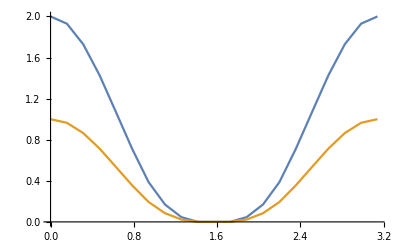

```mathematica
ListLinePlot[{Etmmax,Etmmean}]
```

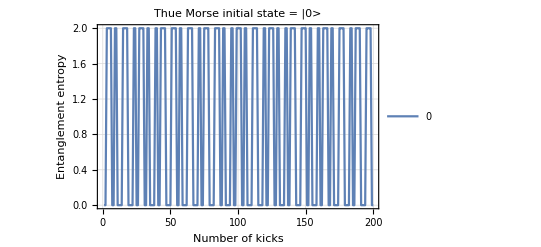

```mathematica
ListLinePlot[Etmn[[1]],PlotTheme->"Detailed",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotLabel->"Thue Morse initial state = |0>",PlotLegends->{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"}, PlotRange->All]
```

## CC Correct (tn dt) dt = pi/8

### data

```mathematica
Etmc={-0.000000000000000000*10^+00,1.201752073385712993*10^+00,2.147215261966105349*10^+00,2.486085893671269531*10^+00,1.613778628454031416*10^+00,1.678645702230858516*10^+00,1.732121179140843736*10^+00,2.809556613000309344*10^+00,2.181937393846531847*10^+00,1.302343840047582413*10^+00,7.727917014037679611*10^-01,1.457836687360993810*10^+00,2.300924172563994397*10^+00,2.878327618070286142*10^+00,2.910099432543583831*10^+00,2.615128085336259289*10^+00,2.334361037919613135*10^+00,2.699593965477515844*10^+00,2.794429893401949805*10^+00,1.833142656531163261*10^+00,6.122243409322629670*10^-01,6.881700381758584228*10^-01,1.869247945024279378*10^+00,2.906516341988083063*10^+00,2.132988547465717311*10^+00,1.591276548828474580*10^+00,1.366310137168003536*10^+00,1.260244333679925832*10^+00,1.704063428493747923*10^+00,2.325459025002965419*10^+00,3.215077001060397510*10^+00,3.672097637728773289*10^+00,3.519756057298293772*10^+00,2.630613588550705817*10^+00,3.024219704383086071*10^+00,3.197487507114621152*10^+00,2.882089146304435801*10^+00,3.003341242565808589*10^+00,2.683662143166831271*10^+00,2.328891458178750540*10^+00,2.917589634090219874*10^+00,3.616084265916592599*10^+00,3.072417492941104111*10^+00,1.962928377334312469*10^+00,1.409519859930277841*10^+00,1.165199811075940728*10^+00,1.738555802683153129*10^+00,2.452380969642273367*10^+00,2.266044032290196242*10^+00,2.269557792034031074*10^+00,1.574024682245550810*10^+00,3.244465836716100560*10^-01,1.072531478996013865*10^+00,1.872164262703995830*10^+00,2.881080578315985186*10^+00,3.055925615844243382*10^+00,3.039165032852077619*10^+00,2.304798988803784532*10^+00,1.794069249908967656*10^+00,2.598206084694725693*10^+00,2.706463613418608638*10^+00,3.490498664409350749*10^+00,2.511486059986022035*10^+00,2.268945096201251399*10^+00,2.753824680624202603*10^+00,2.001925320056910707*10^+00,8.725613255091098086*10^-01,1.918050530792944297*10^+00,2.408634650999772475*10^+00,3.099554428271147799*10^+00,2.332182169965842267*10^+00,2.379523135304276948*10^+00,2.319625228620777690*10^+00,3.042495498497995499*10^+00,2.818353702867710808*10^+00,2.940372450152281658*10^+00,2.352500750022781695*10^+00,1.345105959229794035*10^+00,1.126789589423302373*10^-01,1.320133466346265383*10^+00,2.295502475740282655*10^+00,3.081675176389981008*10^+00,2.652691401434380314*10^+00,2.642438284654604175*10^+00,1.947718246631936045*10^+00,2.314673943665572331*10^+00,1.882206526368319643*10^+00,1.972505572227676085*10^+00,1.208565317256364402*10^+00,2.053573703468374312*10^+00,2.047687808691042832*10^+00,2.081713374421696905*10^+00,1.208489065138414809*10^+00,1.577009894135238399*10^+00,2.300732651042336485*10^+00,3.180227194069466634*10^+00,1.957884184825167129*10^+00,1.537312384745525229*10^+00,1.729133904737581773*10^+00,2.497538146522350733*10^+00,2.313193238742045743*10^+00,2.356506739767892711*10^+00,2.869208649244235687*10^+00,3.210383893680554657*10^+00,3.559226655648974003*10^+00,2.858271997084328220*10^+00,2.883227862804604413*10^+00,2.452835081864127798*10^+00,1.943494277671857562*10^+00,1.710606069626256387*10^+00,1.960276904893991423*10^+00,1.993187135038452684*10^+00,2.252708842054990779*10^+00,1.737394587542528512*10^+00,1.873892164067984867*10^+00,2.672176136196504626*10^+00,2.464572248715009906*10^+00,2.281074191417815200*10^+00,1.926746234931991930*10^+00,2.289045123567655882*10^+00,2.968578555764707527*10^+00,2.621093881237870793*10^+00,3.308365211156790497*10^+00,2.484149289344817824*10^+00,2.644646811762398464*10^+00,2.093673211129314815*10^+00,2.672413544963733401*10^+00,1.859154938912845223*10^+00,2.313839100692204553*10^+00,2.519612956350749222*10^+00,2.092445223685659883*10^+00,2.052180633885311245*10^+00,2.277958240834736969*10^+00,2.573681641687612043*10^+00,2.167239980920238729*10^+00,1.872142663200454749*10^+00,1.611009612339232122*10^+00,1.882202754993783422*10^+00,2.711675698963710524*10^+00,1.898076775253823900*10^+00,2.222923132497051313*10^+00,2.285210097822797604*10^+00,2.632854581797023030*10^+00,2.505658664638937605*10^+00,2.952546952552996373*10^+00,3.485860006688559665*10^+00,2.661744702438054055*10^+00,2.428373829252596927*10^+00,2.089768687279504711*10^+00,2.009187684160486320*10^+00,1.342196911265451043*10^+00,1.460439397900586522*10^+00,1.552531884443933752*10^+00,2.543006490373976192*10^+00,2.040132793001006917*10^+00,9.706258225871410295*10^-01,2.498017422792450370*10^-01,1.501740736983281366*10^+00,2.327592694261271244*10^+00,2.532899704851927503*10^+00,2.015880804039260621*10^+00,1.704191586297671757*10^+00,9.171778875955794996*10^-01,1.997625857438843022*10^+00,2.325666963486748173*10^+00,2.778605373480533824*10^+00,2.454455029839944125*10^+00,3.264740746098786062*10^+00,2.536206819022480463*10^+00,2.840697566064585455*10^+00,2.323107858469530385*10^+00,2.984219828809886899*10^+00,2.521082952620256279*10^+00,2.231387730326212626*10^+00,1.372428709497972577*10^+00,2.065121921558250140*10^+00,2.452718511051823480*10^+00,2.218859007364139657*10^+00,2.534890872622561631*10^+00,2.820361001586291216*10^+00,1.907015586321084255*10^+00,2.067878304485500696*10^+00,1.620845899409668389*10^+00,2.299399413536300951*10^+00,2.398750189309617031*10^+00,2.252444014277387829*10^+00,1.645017825478067852*10^+00,1.552687157185705491*10^+00,1.512304891389844030*10^+00,1.486441892923878294*10^+00,2.409067732783779725*10^+00,3.079136655225540142*10^+00,2.533824947892973967*10^+00,2.651254588505347343*10^+00,1.872677762966052928*10^+00,1.477214541470441178*10^+00,1.545043138512784076*10^+00,1.575366940417504136*10^+00,2.584007363117533984*10^+00,3.443074434279193241*10^+00,2.722912528242654327*10^-14,1.201752073385711883*10^+00,2.130597445629470954*10^+00,2.457408176232198205*10^+00,1.608756058568337144*10^+00,1.676443671583761397*10^+00,1.799584383529011511*10^+00,2.797493518254231315*10^+00,2.190068943262494905*10^+00,1.293826784258075513*10^+00,7.424678263951569601*10^-01,1.399972758088792402*10^+00,2.229779085019085727*10^+00,2.808992134877875024*10^+00,2.833826706840112841*10^+00,2.553951719906247142*10^+00,2.244155712654317014*10^+00,2.634057272275294626*10^+00,2.696204279988042796*10^+00,1.875072540763037754*10^+00,6.783690277407137259*10^-01,7.654837078193900135*10^-01,1.940627271750602123*10^+00,2.899651746916481976*10^+00,2.139997816340281300*10^+00,1.609645013935941726*10^+00,1.417803094598910629*10^+00,1.368250622396346428*10^+00,1.781906630808712588*10^+00,2.359064240132055179*10^+00,3.191823974670200403*10^+00,3.611100083195909249*10^+00,3.385550582828322774*10^+00,2.509813055111200342*10^+00,2.947470631017599541*10^+00,3.177450628582121350*10^+00,2.929992084918445094*10^+00,3.048603028024138517*10^+00,2.836145466378416469*10^+00,2.518166253996955373*10^+00,2.985347349620606217*10^+00,3.573205833160267186*10^+00,3.092253026411818873*10^+00,2.221741803638328960*10^+00,1.711852761240598930*10^+00,1.480925646354497305*10^+00,2.004876761694622811*10^+00,2.664307336325067332*10^+00,2.456379136118199025*10^+00,2.423598344581364028*10^+00,1.860493909300536375*10^+00,6.709097103085257530*10^-01,1.354801275513081382*10^+00,2.101345888331091594*10^+00,3.019738167390106032*10^+00,3.173345161223000588*10^+00,3.180785401085099551*10^+00,2.486195022548180589*10^+00,2.009216685448590223*10^+00,2.743842475563122552*10^+00,2.839827457933655097*10^+00,3.505743274478116511*10^+00,2.543508563389011989*10^+00,2.315093803961554286*10^+00,2.795665089656196312*10^+00,2.130703159753909226*10^+00,1.139079821462325670*10^+00,2.093777487253826397*10^+00,2.502750321712537751*10^+00,3.157413737959647193*10^+00,2.493771999032337483*10^+00,2.491832519545587932*10^+00,2.373674463438581128*10^+00,3.015963104102976633*10^+00,2.868551458540146371*10^+00,3.051446841936903187*10^+00,2.522471603888503555*10^+00,1.628070962974800695*10^+00,4.653545153278737523*10^-01,1.573137067812398815*10^+00,2.476868509172603705*10^+00,3.158114645997189385*10^+00,2.799842544488116758*10^+00,2.792715229691386636*10^+00,2.165483457839946002*10^+00,2.533451191227575006*10^+00,2.151446559106099610*10^+00,2.206413895604758757*10^+00,1.420188891586298352*10^+00,2.262899296509495173*10^+00,2.275842004534697427*10^+00,2.327242148897977980*10^+00,1.518369593095736159*10^+00,1.858342614868360609*10^+00,2.498027854341376308*10^+00,3.252206255364361365*10^+00,2.248348574129749977*10^+00,1.807536746616328793*10^+00,1.974170076419175412*10^+00,2.647365105186842982*10^+00,2.481951534577402363*10^+00,2.515145878391191747*10^+00,2.924622834637069957*10^+00,3.206938273231886072*10^+00,3.575914579276755489*10^+00,2.993776614372110068*10^+00,2.987817592092405050*10^+00,2.522939246821428227*10^+00,2.021552541070847031*10^+00,1.788451272687070936*10^+00,1.975210763496798139*10^+00,2.010325998632741751*10^+00,2.288827840941059399*10^+00,1.851111716152480824*10^+00,1.954529532662628633*10^+00,2.628324055187253094*10^+00,2.449850264226994145*10^+00,2.367189484733317251*10^+00,2.058003228948086072*10^+00,2.378958493285147746*10^+00,3.004096464890932516*10^+00,2.706449023742428572*10^+00,3.367391330855545650*10^+00,2.609967424633801159*10^+00,2.705464567235241535*10^+00,2.197631305232950361*10^+00,2.687260041289134982*10^+00,1.906995733035239171*10^+00,2.358709572778093566*10^+00,2.578199012818533475*10^+00,2.140348751284365747*10^+00,2.039845855897233662*10^+00,2.247527214151146424*10^+00,2.567263303269196051*10^+00,2.207516933091135947*10^+00,1.914700751293744396*10^+00,1.691615104232937039*10^+00,1.976488622673381101*10^+00,2.773165464668896796*10^+00,2.049047655046031924*10^+00,2.346106492286819112*10^+00,2.408561374852102865*10^+00,2.737660609020799551*10^+00,2.532576970444376130*10^+00,2.962108922409617762*10^+00,3.426933869751703110*10^+00,2.658547774692749499*10^+00,2.389964493560969405*10^+00,2.078564655115763937*10^+00,2.014632557330400697*10^+00,1.350790851729190223*10^+00,1.434597089357643407*10^+00,1.554418715860816924*10^+00,2.469470922339757735*10^+00,2.107338734536664315*10^+00,1.143781404138209057*10^+00,4.862727135976108173*10^-01,1.651674123085586476*10^+00,2.336695103616826863*10^+00,2.582392247141421127*10^+00,2.123171915228187157*10^+00,1.845778094796216573*10^+00,1.064077897539977391*10^+00,2.065988277812019547*10^+00,2.364806030094047884*10^+00,2.786957748437070226*10^+00,2.472568575167284788*10^+00,3.199315889127261059*10^+00,2.481220415228257536*10^+00,2.779859700273800360*10^+00,2.348054258724245891*10^+00,2.981667764137349241*10^+00,2.522681009964775178*10^+00,2.253029680291726677*10^+00,1.449869430220791289*10^+00,2.107391915693565210*10^+00,2.454059643948685920*10^+00,2.207605956536684122*10^+00,2.516520154855486524*10^+00,2.878487159724201216*10^+00,2.083396641607537347*10^+00,2.231724094726603713*10^+00,1.874729552354298168*10^+00,2.473533554635882759*10^+00,2.527759569182164601*10^+00,2.395036362213121883*10^+00,1.892651124068594370*10^+00,1.814111052178844607*10^+00,1.753248011773095971*10^+00,1.689947963542398179*10^+00,2.503235457895569560*10^+00,3.170219179778718033*10^+00,2.637351470562365741*10^+00,2.699576704056173782*10^+00,1.989584157874480619*10^+00,1.659628546483944422*10^+00,1.745224848736036227*10^+00,1.766941774405840437*10^+00,2.717024336107741966*10^+00,3.504364194251772258*10^+00,-9.610279511444755881*10^-16,1.201752073385713659*10^+00,2.083205861098788247*10^+00,2.376385127585977308*10^+00,1.569153374220666253*10^+00,1.669494184133583303*10^+00,1.876320343496409526*10^+00,2.772476073231956217*10^+00,2.224989076417945189*10^+00,1.306765430068862255*10^+00,7.226720479474892933*10^-01,1.309480267890797744*10^+00,2.090678474420981203*10^+00,2.687528512840555273*10^+00,2.703154954356092432*10^+00,2.431871912345408226*10^+00,2.031346648454262827*10^+00,2.438236776216158752*10^+00,2.406279925401559883*10^+00,1.869063691944480965*10^+00,8.631475874521510327*10^-01,9.636616830808877321*10^-01,2.053420455687716917*10^+00,2.877140927708575990*10^+00,2.167519709196275013*10^+00,1.665991347083273677*10^+00,1.559242489338760196*10^+00,1.628895253327355075*10^+00,1.986052152548042349*10^+00,2.447273890972599730*10^+00,3.159071037542728000*10^+00,3.464825758731878036*10^+00,3.059683560676994762*10^+00,2.268872416123116409*10^+00,2.760340726853200088*10^+00,3.146175615867606190*10^+00,3.028270901803817416*10^+00,3.108381356861253941*10^+00,3.105375549416646397*10^+00,2.809715203583211363*10^+00,3.154541123722040652*10^+00,3.484119569220545554*10^+00,3.152012936363213225*10^+00,2.589412286771068494*10^+00,2.203331493938382124*10^+00,2.006359256974090233*10^+00,2.388031604303521682*10^+00,2.932567079046603187*10^+00,2.702504843676679425*10^+00,2.648087737754674098*10^+00,2.343286494141481935*10^+00,1.272993552636732417*10^+00,1.831300297097346430*10^+00,2.462262245695975071*10^+00,3.173129586281591585*10^+00,3.292586277730854771*10^+00,3.371899267821040880*10^+00,2.770142513397650053*10^+00,2.312919993359598525*10^+00,2.920958871380085586*10^+00,2.943122031441387509*10^+00,3.471378827348645224*10^+00,2.569261925103784705*10^+00,2.429916326966368167*10^+00,2.841029334150089625*10^+00,2.322393058421756251*10^+00,1.598862782760306800*10^+00,2.366796232431851443*10^+00,2.633984535978146191*10^+00,3.208063168440895563*10^+00,2.784906573267305507*10^+00,2.681061435011737881*10^+00,2.509301089114845507*10^+00,2.957775864198945115*10^+00,3.016396812698352470*10^+00,3.214380974933188639*10^+00,2.790121012938746592*10^+00,2.083072588673339887*10^+00,1.133559173013546140*10^+00,1.945254114095021691*10^+00,2.704688017877098005*10^+00,3.278848668478226092*10^+00,2.974637356535557942*10^+00,2.951649170245926435*10^+00,2.415000738843500194*10^+00,2.833381774128516994*10^+00,2.562496214802641781*10^+00,2.533209525012557251*10^+00,1.740478283340694210*10^+00,2.515549446206976292*10^+00,2.551879222757357013*10^+00,2.668679998331354497*10^+00,2.035525773128056493*10^+00,2.333077321059952247*10^+00,2.865315116210155999*10^+00,3.411289799514721111*10^+00,2.663723260914230728*10^+00,2.186658944072013444*10^+00,2.318817932988372021*10^+00,2.902062535723058723*10^+00,2.792213949967537800*10^+00,2.802942414425744211*10^+00,3.050814467244974182*10^+00,3.188669317906309253*10^+00,3.554655782688350030*10^+00,3.168089809749257135*10^+00,3.144993281098095395*10^+00,2.650337416013777592*10^+00,2.177637725115530110*10^+00,1.953225978081283509*10^+00,2.018472725171809312*10^+00,2.079141211097399466*10^+00,2.378914064696139086*10^+00,2.091821852757343780*10^+00,2.143444527667449861*10^+00,2.575258883790990438*10^+00,2.456397195253973820*10^+00,2.550725935083035800*10^+00,2.296637093331742818*10^+00,2.542313896692179220*10^+00,3.058741480469047591*10^+00,2.842993818814163909*10^+00,3.423207964852093443*10^+00,2.796973037717127131*10^+00,2.749879748329161266*10^+00,2.300120881768228376*10^+00,2.691647826434058199*10^+00,2.063505084870459694*10^+00,2.476256264526190964*10^+00,2.688845252920001094*10^+00,2.252341129086497418*10^+00,2.040980053171824071*10^+00,2.170735259742138545*10^+00,2.556347001659271534*10^+00,2.303875059078821508*10^+00,2.024652107628506670*10^+00,1.872055480377336378*10^+00,2.123731091174941188*10^+00,2.827213683089937479*10^+00,2.348031197484048427*10^+00,2.575845360725815603*10^+00,2.643057212944286416*10^+00,2.938504892012541170*10^+00,2.593099759454540632*10^+00,2.985035472028180870*10^+00,3.284292879857440450*10^+00,2.640042811474794249*10^+00,2.307439851274025511*10^+00,2.074933149433213941*10^+00,2.068836165089094070*10^+00,1.474547342394115557*10^+00,1.403897964970769241*10^+00,1.496192436032070194*10^+00,2.356181126472355114*10^+00,2.287867270970301181*10^+00,1.521908664547481083*10^+00,1.009763632449981241*10^+00,1.863884133237567520*10^+00,2.307267403668184613*10^+00,2.627112385750149048*10^+00,2.332245364888752448*10^+00,2.120603517900775170*10^+00,1.380392483343773513*10^+00,2.204449415059452022*10^+00,2.431504784115085638*10^+00,2.806055385202092634*10^+00,2.514081460764459486*10^+00,3.030190508219012813*10^+00,2.334481071722453116*10^+00,2.662074269841867569*10^+00,2.398290189905343706*10^+00,2.967448332510835840*10^+00,2.496418710988837386*10^+00,2.247082647328333405*10^+00,1.576758721477401481*10^+00,2.218979663609487396*10^+00,2.436346163741032633*10^+00,2.154085376941499153*10^+00,2.466436183770936097*10^+00,2.977228664424536930*10^+00,2.437046132404920851*10^+00,2.551097235722157741*10^+00,2.326210681506376332*10^+00,2.748777939829804673*10^+00,2.764616073798307205*10^+00,2.694911963912993258*10^+00,2.386720854673604286*10^+00,2.276123921971886510*10^+00,2.130601538625375824*10^+00,2.054995849784075013*10^+00,2.664676007764368748*10^+00,3.302829140390489471*10^+00,2.794482548681277656*10^+00,2.773067195977177768*10^+00,2.205988799291945579*10^+00,1.983502699413054682*10^+00,2.046083747275623921*10^+00,2.113617974397336230*10^+00,2.886032475968820066*10^+00,3.550482005873804692*10^+00,9.610279511444749964*10^-16,1.201752073385712993*10^+00,2.011928759656730126*10^+00,2.257372989934149032*10^+00,1.536034111857915718*10^+00,1.665422429914332314*10^+00,1.965248436599643433*10^+00,2.747860617199101352*10^+00,2.288055307784970793*10^+00,1.470403792962157397*10^+00,8.126227953418921901*10^-01,1.346675331546436372*10^+00,2.055500411438850872*10^+00,2.629650046941002461*10^+00,2.655594727028526059*10^+00,2.364086914314699417*10^+00,1.800058237527507377*10^+00,2.124793795861368739*10^+00,1.998085552250403296*10^+00,1.763802669136211199*10^+00,1.033155261006494907*10^+00,1.167727046069666041*10^+00,2.141023052407926563*10^+00,2.853368734726397182*10^+00,2.228041347019138030*10^+00,1.765880383611737381*10^+00,1.768397150377002847*10^+00,1.984844905454303365*10^+00,2.274418676036788600*10^+00,2.557965836554732419*10^+00,3.109053839258293372*10^+00,3.297453211995852396*10^+00,2.746196007438792996*10^+00,2.046906405084564895*10^+00,2.571866778286512556*10^+00,3.128187055138550665*10^+00,3.105236940521049149*10^+00,3.112785426200600725*10^+00,3.291104367681144449*10^+00,2.965834725738985433*10^+00,3.331051711474065868*10^+00,3.392732595548531904*10^+00,3.214732232086709107*10^+00,2.882071960241411102*10^+00,2.601722340264538413*10^+00,2.409529772654254387*10^+00,2.597984509608900261*10^+00,3.033198410339655648*10^+00,2.835145434130445175*10^+00,2.780451702216228060*10^+00,2.764306114082558885*10^+00,1.895717058667796939*10^+00,2.234681137418159214*10^+00,2.697862331680960679*10^+00,3.174802993860259992*10^+00,3.249505474867590227*10^+00,3.409461521801899764*10^+00,2.961013217197386638*10^+00,2.529460771245224393*10^+00,2.935656386546596774*10^+00,2.861514887540124175*10^+00,3.316797616125080062*10^+00,2.578655181839953237*10^+00,2.537118266071293426*10^+00,2.787010829565999437*10^+00,2.413853817948047986*10^+00,1.942498576155067269*10^+00,2.499479587661493252*10^+00,2.649901371613545553*10^+00,3.147017659362979281*10^+00,3.037697461305399749*10^+00,2.846087123611081626*10^+00,2.664974519161012356*10^+00,2.891571352095088532*10^+00,3.121626926824569992*10^+00,3.264918191392427005*10^+00,3.012451835427132352*10^+00,2.474984171521230625*10^+00,1.784345759311470214*10^+00,2.255316076759561916*10^+00,2.819370473193860249*10^+00,3.317888954420315173*10^+00,3.012741398348889543*10^+00,2.972102828036639721*10^+00,2.529170176390688418*10^+00,2.989464940216536526*10^+00,2.846912343083902286*10^+00,2.722468352768192101*10^+00,1.938679870467422850*10^+00,2.625684393750256085*10^+00,2.703110720129338507*10^+00,2.884278653011542293*10^+00,2.426213315214553745*10^+00,2.694395771322763977*10^+00,3.099400836252302227*10^+00,3.499545708756191864*10^+00,2.911727088239569383*10^+00,2.459568072046114384*10^+00,2.549717251472814361*10^+00,3.053170797143005544*10^+00,3.042305422425524597*10^+00,3.015111927790270041*10^+00,3.149961348720641041*10^+00,3.128789835451785795*10^+00,3.416834689412835857*10^+00,3.212054122738038586*10^+00,3.223221057702211567*10^+00,2.772404517619848630*10^+00,2.386691118674777901*10^+00,2.099501773641244462*10^+00,2.086491270617421900*10^+00,2.181102104790387575*10^+00,2.562317799491251158*10^+00,2.350043884028020891*10^+00,2.367472357783142911*10^+00,2.558783665521787043*10^+00,2.497557538340640537*10^+00,2.734719516777345039*10^+00,2.504634498911872953*10^+00,2.655498311489606245*10^+00,3.054594934776435622*10^+00,2.920443861168705357*10^+00,3.371110147449849492*10^+00,2.891324186549849351*10^+00,2.693384316644430676*10^+00,2.319653318067594228*10^+00,2.670055200212611446*10^+00,2.297491028268423996*10^+00,2.623475328838646981*10^+00,2.840430679452968121*10^+00,2.329389565596818201*10^+00,2.052047772202092446*10^+00,2.153268057088338683*10^+00,2.570476955925398599*10^+00,2.392931161901787895*10^+00,2.147640312437248955*10^+00,2.094061658053103514*10^+00,2.237454468331892432*10^+00,2.785778434219797095*10^+00,2.595116573314121489*10^+00,2.753527562352001024*10^+00,2.840600963851245275*10^+00,3.095660264826050945*10^+00,2.663132678988651580*10^+00,3.022312848053994472*10^+00,3.111814100156755192*10^+00,2.595262966605970778*10^+00,2.241383101124786670*10^+00,2.145685785536280754*10^+00,2.221986056130420106*10^+00,1.687847701208351925*10^+00,1.468458760917344064*10^+00,1.501713301273042367*10^+00,2.324217914179946831*10^+00,2.470690371172914901*10^+00,1.901137772227996514*10^+00,1.495042617170804222*10^+00,1.981528250873366925*10^+00,2.180791828744002903*10^+00,2.541776163204761740*10^+00,2.464456169884330805*10^+00,2.351347575247049626*10^+00,1.728379307699978051*10^+00,2.319322299011857602*10^+00,2.466634792432120360*10^+00,2.815513679330286401*10^+00,2.547615328970501025*10^+00,2.819973944050822912*10^+00,2.172299823619751713*10^+00,2.526026762562273653*10^+00,2.433745760706292671*10^+00,2.922736251115980455*10^+00,2.411841692121740266*10^+00,2.151236566194340671*10^+00,1.621059450323412809*10^+00,2.227527755197934667*10^+00,2.363746457138433676*10^+00,2.041638559628706329*10^+00,2.397519297761505186*10^+00,3.042898078548912810*10^+00,2.714563302678377088*10^+00,2.790871336259131308*10^+00,2.720376908189269471*10^+00,2.895744815596644095*10^+00,2.933924070147821972*10^+00,2.919717261337022141*10^+00,2.831392482156317669*10^+00,2.671424422836643053*10^+00,2.448096588544365293*10^+00,2.334972650788007087*10^+00,2.696884769169542118*10^+00,3.313976354915191269*10^+00,2.847306241312492325*10^+00,2.780496107320491905*10^+00,2.361365737296575951*10^+00,2.201893710433810547*10^+00,2.252348117098586844*10^+00,2.354797728599765438*10^+00,2.916401631066062983*10^+00,3.457443751303209023*10^+00,4.805139755722374982*10^-16,1.201752073385712549*10^+00,1.926685354281866935*10^+00,2.112357066224149538*10^+00,1.511656856450188435*10^+00,1.677477782384769966*10^+00,2.020144179860876577*10^+00,2.743876476231131178*10^+00,2.358603804958145478*10^+00,1.722635127266462396*10^+00,1.052200735372847529*10^+00,1.579725034160978758*10^+00,2.168739568833360387*10^+00,2.641402034639694030*10^+00,2.655993711452009798*10^+00,2.365370695443553384*10^+00,1.657498480404931085*10^+00,1.829193443506119010*10^+00,1.627096404858002998*10^+00,1.637006361540682464*10^+00,1.223741966019966876*10^+00,1.367536897236922400*10^+00,2.227796075422676214*10^+00,2.852297281560960407*10^+00,2.335023471831134678*10^+00,1.940862596733426981*10^+00,2.007492812251668202*10^+00,2.297403812779920784*10^+00,2.539913837739617541*10^+00,2.636523582120962050*10^+00,3.006610593163244527*10^+00,3.171841461667760598*10^+00,2.645804998315305578*10^+00,1.990584167918371783*10^+00,2.504898361658105532*10^+00,3.118738993267943016*10^+00,3.174390003075129751*10^+00,3.085103729883299284*10^+00,3.340565073968258414*10^+00,3.007281969246668574*10^+00,3.426414401743842930*10^+00,3.316181327729585515*10^+00,3.220814857348954341*10^+00,3.044896824269232027*10^+00,2.817133055697957467*10^+00,2.582673299186704075*10^+00,2.586125816121171539*10^+00,2.960357625237904244*10^+00,2.874170465389894069*10^+00,2.931040824187015836*10^+00,3.043344125193044647*10^+00,2.404743084092992866*10^+00,2.528529813332235587*10^+00,2.848371617644738230*10^+00,3.094864047373496074*10^+00,3.123959743886339346*10^+00,3.318500869359236827*10^+00,3.047998480191258519*10^+00,2.693067472199076828*10^+00,2.833773644245801915*10^+00,2.666027492935152399*10^+00,3.118853642013815097*10^+00,2.607852780559430261*10^+00,2.632181789133730021*10^+00,2.706130856213100788*10^+00,2.359662315886316808*10^+00,2.051395385199946020*10^+00,2.425848970793301529*10^+00,2.551903507605663979*10^+00,3.040003077500316842*10^+00,3.251773633971779986*10^+00,3.005580827009367795*10^+00,2.794056381044264903*10^+00,2.851216944902684958*10^+00,3.111726928135311709*10^+00,3.199751285729839356*10^+00,3.135041151920785918*10^+00,2.745127189111316035*10^+00,2.260191378496116510*10^+00,2.487158750804637108*10^+00,2.860761990537201704*10^+00,3.264568711383053490*10^+00,2.899475882168235152*10^+00,2.878131407488246918*10^+00,2.597408305503755788*10^+00,3.031723477934359590*10^+00,2.959511232115014767*10^+00,2.846319636730811009*10^+00,2.128933535330983950*10^+00,2.703858706647675358*10^+00,2.790632600267799468*10^+00,3.009474357962720781*10^+00,2.660545636687607018*10^+00,2.855800236418582827*10^+00,3.161070972902769949*10^+00,3.441890533693515497*10^+00,3.005217204610033832*10^+00,2.631385064057992107*10^+00,2.699945637308690749*10^+00,3.055411277552551041*10^+00,3.117605605934258506*10^+00,3.047607375549602260*10^+00,3.137464388210142729*10^+00,3.006730902118693649*10^+00,3.191744076465703905*10^+00,3.148725428253939640*10^+00,3.240088427106873947*10^+00,2.935638647266249013*10^+00,2.655671805086088355*10^+00,2.259502053277249622*10^+00,2.217459616084275442*10^+00,2.336534724421593268*10^+00,2.754257706398841599*10^+00,2.598912521026117695*10^+00,2.576556328934820783*10^+00,2.548722778634819441*10^+00,2.555036499029945674*10^+00,2.857345318606372864*10^+00,2.630797971681166025*10^+00,2.652815697558259522*10^+00,2.956156556458382489*10^+00,2.907735984136099461*10^+00,3.241192966077142135*10^+00,2.898348087480578705*10^+00,2.591959668432612052*10^+00,2.292877708486873445*10^+00,2.623504083087811356*10^+00,2.566080615778568941*10^+00,2.847961660256320027*10^+00,2.952594012250349120*10^+00,2.358493670363618122*10^+00,2.110882083738510495*10^+00,2.243069055205110907*10^+00,2.644368671338791721*10^+00,2.426946920114724904*10^+00,2.233700851157281342*10^+00,2.259597411588306404*10^+00,2.270207032452429274*10^+00,2.620892529711819297*10^+00,2.705595367620852620*10^+00,2.835483014051521700*10^+00,2.952136962060620373*10^+00,3.151306220238286215*10^+00,2.744358245222298542*10^+00,3.099915921298824539*10^+00,2.977515474430438402*10^+00,2.521331750534417715*10^+00,2.265039270778952396*10^+00,2.320990353208204571*10^+00,2.465299075016586183*10^+00,1.943793323492958525*10^+00,1.611861117229452356*10^+00,1.608654704141224689*10^+00,2.366051861740812612*10^+00,2.621546235547205672*10^+00,2.135460327556047755*10^+00,1.763723320296679553*10^+00,1.936003248725514103*10^+00,2.000653547826017231*10^+00,2.348856364264547913*10^+00,2.465200867501435855*10^+00,2.515567048779895565*10^+00,2.065862347121139031*10^+00,2.395158497196548719*10^+00,2.472671932210391610*10^+00,2.813403282040938702*10^+00,2.549989615829018064*10^+00,2.635130782175560515*10^+00,2.046075058595789198*10^+00,2.435760728672187625*10^+00,2.438767317169933335*10^+00,2.848518492516797451*10^+00,2.315857828636900706*10^+00,2.030230731182157022*10^+00,1.655558469724403015*10^+00,2.145345956855311709*10^+00,2.207950141382413189*10^+00,1.921394914365671003*10^+00,2.372622291930810867*10^+00,3.062163128811421942*10^+00,2.907402106147942256*10^+00,2.898812758958354330*10^+00,2.950570321548209751*10^+00,2.911703434916636191*10^+00,2.983694769937049962*10^+00,2.984946201895151585*10^+00,3.071124845065595910*10^+00,2.901204799277839363*10^+00,2.650298260991878152*10^+00,2.472682070600766835*10^+00,2.587375541197443063*10^+00,3.184775052673611828*10^+00,2.797253591874927281*10^+00,2.728821139255917849*10^+00,2.554103224650700277*10^+00,2.372936024433216051*10^+00,2.388090380335731844*10^+00,2.452965287157115704*10^+00,2.837608091780942310*10^+00,3.279237153956304773*10^+00,3.203426503814917641*10^-16,1.201752073385712549*10^+00,1.838431230982315867*10^+00,1.988638394604741455*10^+00,1.560298586395604481*10^+00,1.720966473360169058*10^+00,2.035322578519477510*10^+00,2.717971792775751183*10^+00,2.355480362108931303*10^+00,1.925647474003250981*10^+00,1.360205360313685663*10^+00,1.895663877211399395*10^+00,2.320734100848945936*10^+00,2.614443769117530625*10^+00,2.625758958227913276*10^+00,2.364141005696909659*10^+00,1.599382926325267240*10^+00,1.680866174386570933*10^+00,1.510698305092026406*10^+00,1.644106463520115691*10^+00,1.456812080048458746*10^+00,1.599942385824974167*10^+00,2.319109844687067490*10^+00,2.872646179412607470*10^+00,2.439053018001723583*10^+00,2.146269504809168449*10^+00,2.221279067196595403*10^+00,2.501832231213625857*10^+00,2.689554686558558672*10^+00,2.635186588823826614*10^+00,2.884170970871910544*10^+00,3.109521736689241589*10^+00,2.749075063696748700*10^+00,2.106987492581201771*10^+00,2.505702436710509851*10^+00,3.093824804807341344*10^+00,3.270232702375902356*10^+00,3.070141504344012340*10^+00,3.327810037223257744*10^+00,3.054591730331941868*10^+00,3.424769175199838589*10^+00,3.233042017997096451*10^+00,3.204495204151144971*10^+00,3.077574291054284927*10^+00,2.883245554260952748*10^+00,2.566970296719746081*10^+00,2.428966102293106388*10^+00,2.844681761346237181*10^+00,2.970457485529334196*10^+00,3.118215555962735142*10^+00,3.185399019787402253*10^+00,2.735354523807601357*10^+00,2.736814093691811944*10^+00,2.959304599795502977*10^+00,3.049959690182987959*10^+00,3.004853493020418043*10^+00,3.199640144295234023*10^+00,3.085529885383286430*10^+00,2.784808958375740495*10^+00,2.710712702613927938*10^+00,2.468800616158682182*10^+00,2.980669823879955160*10^+00,2.716320941043681714*10^+00,2.772045858228104009*10^+00,2.627230211926708137*10^+00,2.205397859670414462*10^+00,1.961618745793660690*10^+00,2.238323161218335855*10^+00,2.457309617297316340*10^+00,2.985100827536183665*10^+00,3.384246900417025916*10^+00,3.164325570911202590*10^+00,2.912839743967468475*10^+00,2.836821110630755705*10^+00,3.028945674776337249*10^+00,3.108526215495261091*10^+00,3.215700012472384905*10^+00,2.906639046440676388*10^+00,2.553794818690086732*10^+00,2.633924583630662841*10^+00,2.896454513703915712*10^+00,3.162026440673642913*10^+00,2.741978285893427181*10^+00,2.769224713356815748*10^+00,2.694098822959990258*10^+00,3.040276612438566950*10^+00,2.981332577245352500*10^+00,2.959663296152339029*10^+00,2.428995553179440492*10^+00,2.881986765852541765*10^+00,2.908534396627159069*10^+00,3.055565458485607344*10^+00,2.776064521684409314*10^+00,2.856395282322536033*10^+00,3.079576887783028738*10^+00,3.261031841915380092*10^+00,2.975750346459563378*10^+00,2.763760472969188697*10^+00,2.822404368298241817*10^+00,2.965919939141368200*10^+00,3.034328474605039627*10^+00,2.935563063913039006*10^+00,3.038950224505686748*10^+00,2.839430900365648824*10^+00,2.977252195291017145*10^+00,3.065059761681406592*10^+00,3.238495351853733606*10^+00,3.154788315135678811*10^+00,2.961415660547502160*10^+00,2.487625843254055891*10^+00,2.422913913334867608*10^+00,2.555363138597207318*10^+00,2.926195631034613776*10^+00,2.809680249927942519*10^+00,2.757873208214758787*10^+00,2.540690101997380435*10^+00,2.603659493392034285*10^+00,2.900841787641244007*10^+00,2.662939242797038641*10^+00,2.517894560805515436*10^+00,2.761739444232869989*10^+00,2.815119957978925225*10^+00,3.095603487421385580*10^+00,2.880165549947256487*10^+00,2.564796741182071571*10^+00,2.292177075518602614*10^+00,2.593735649949812760*10^+00,2.795572874358005944*10^+00,3.007904664445153475*10^+00,2.998982889992457324*10^+00,2.366265327175521183*10^+00,2.226071360854985581*10^+00,2.422827664313223384*10^+00,2.723013977356451232*10^+00,2.459019891499956145*10^+00,2.306336909105925592*10^+00,2.340131150512722691*10^+00,2.219120595541002494*10^+00,2.403800882712868070*10^+00,2.708191227857423389*10^+00,2.839542050760099912*10^+00,3.001450615113359977*10^+00,3.141399092405618987*10^+00,2.862752063229216049*10^+00,3.225638606505082162*10^+00,2.961911430689193381*10^+00,2.491083785034456710*10^+00,2.373287270093530577*10^+00,2.563325081395748661*10^+00,2.704765369427855504*10^+00,2.170993779361976017*10^+00,1.749672212356946144*10^+00,1.747468979563451930*10^+00,2.434908040716797561*10^+00,2.694693412653374587*10^+00,2.161474910144356887*10^+00,1.825631782042989926*10^+00,1.805041844781048788*10^+00,1.866748642931244317*10^+00,2.121305628705057345*10^+00,2.360782998630596818*10^+00,2.625263891758454093*10^+00,2.359540154234140541*10^+00,2.444454289488343868*10^+00,2.494083697305828906*10^+00,2.807286110503426357*10^+00,2.563344820156498116*10^+00,2.512950649375595535*10^+00,2.002726860760515315*10^+00,2.427758000953644135*10^+00,2.426444094429447862*10^+00,2.764671817539039012*10^+00,2.299214494353033711*10^+00,1.999323573932063836*10^+00,1.725122226317403529*10^+00,2.151483454162549158*10^+00,2.132600434802687683*10^+00,1.931494188428160230*10^+00,2.375024216067387783*10^+00,3.049049354352295627*10^+00,3.041538976979862863*10^+00,2.942174912302471412*10^+00,3.039540121396601791*10^+00,2.865710664553998033*10^+00,2.965572655462049845*10^+00,2.934654545964367145*10^+00,3.107838463079953151*10^+00,2.979091259073904041*10^+00,2.711743509057723323*10^+00,2.455391276304828896*10^+00,2.380274264927384475*10^+00,2.976854819608093727*10^+00,2.733484205493565078*10^+00,2.712952143015654016*10^+00,2.746718222748544491*10^+00,2.588901923774551417*10^+00,2.482630830621260554*10^+00,2.516761881302893578*10^+00,2.762111669231102073*10^+00,3.115438428329186493*10^+00,-9.610279511444755881*10^-16,1.201752073385711883*10^+00,1.738111176542852743*10^+00,1.903314481967259164*10^+00,1.674941995097545266*10^+00,1.788747693178664777*10^+00,2.048673500413654480*10^+00,2.627847983135851440*10^+00,2.268367699935073478*10^+00,2.007808265647239576*10^+00,1.667639112563586545*10^+00,2.188508960753261956*10^+00,2.483489901567228486*10^+00,2.554435975234464085*10^+00,2.538339689158277679*10^+00,2.347250340867118812*10^+00,1.634806276445918582*10^+00,1.725852254838956545*10^+00,1.728612870974918225*10^+00,1.831117650444181510*10^+00,1.759799269851382020*10^+00,1.827200801955024545*10^+00,2.395279516729736713*10^+00,2.814250682497766665*10^+00,2.474009225832832115*10^+00,2.344550570130602196*10^+00,2.371130458776928407*10^+00,2.564504550317248555*10^+00,2.688452374837037695*10^+00,2.529805522403371310*10^+00,2.740553192804599192*10^+00,3.132512057934664362*10^+00,2.812036228904657875*10^+00,2.197445821467889360*10^+00,2.444756019376464806*10^+00,3.026939802732043994*10^+00,3.319529889697554914*10^+00,3.061570178578446377*10^+00,3.303357193482305831*10^+00,3.134793139528206041*10^+00,3.340838913755265427*10^+00,3.109736609037970556*10^+00,3.122158338404423805*10^+00,3.044067001480323054*10^+00,2.838540771183790667*10^+00,2.462443955882327451*10^+00,2.257983672893323135*10^+00,2.773549384495037184*10^+00,3.071556070336491917*10^+00,3.230840684271192309*10^+00,3.251831227772501887*10^+00,2.922436573656075787*10^+00,2.870971793922139081*10^+00,3.059632564023110568*10^+00,3.077916428346948230*10^+00,2.941813286476171463*10^+00,3.112774283247797591*10^+00,3.072690567450581334*10^+00,2.839515037106967288*10^+00,2.607332939920587123*10^+00,2.323780187872487080*10^+00,2.910593458402566558*10^+00,2.885219015816368415*10^+00,2.895121086494007123*10^+00,2.597945520854179513*10^+00,2.046093612038496268*10^+00,1.784008304880193796*10^+00,2.064466558677223951*10^+00,2.444326642920089832*10^+00,2.997353703144542081*10^+00,3.445760804277690159*10^+00,3.275805530116036479*10^+00,3.006498366957590207*10^+00,2.830254254221348909*10^+00,2.935310559138984310*10^+00,3.066009726441326855*10^+00,3.237632372962677696*10^+00,2.991484467076866771*10^+00,2.702068836126221729*10^+00,2.700707198348208493*10^+00,2.932973727599597513*10^+00,3.052390335937602561*10^+00,2.638626014738497894*10^+00,2.683358324996836242*10^+00,2.838254598886270408*10^+00,3.050850224061923299*10^+00,2.968972577633545384*10^+00,3.061052458085095740*10^+00,2.712005395841255329*10^+00,3.133056111725921689*10^+00,3.107098656424010397*10^+00,3.102982171424572222*10^+00,2.827306451151701427*10^+00,2.779538905124696591*10^+00,2.952030430400213845*10^+00,3.006841039141253447*10^+00,2.887157951532095090*10^+00,2.868172612216011608*10^+00,2.908094407044994334*10^+00,2.872463743676056946*10^+00,2.898744843589628140*10^+00,2.780130967213131132*10^+00,2.941079921662276053*10^+00,2.746165455536288658*10^+00,2.890813874603855638*10^+00,2.993946723122622444*10^+00,3.249681764904226000*10^+00,3.407236231987818886*10^+00,3.291505827655254457*10^+00,2.709284882342252843*10^+00,2.645402113892053375*10^+00,2.763606087616893081*10^+00,3.043481708795030549*10^+00,2.985803502423743261*10^+00,2.865564385078493981*10^+00,2.515739765559658725*10^+00,2.615617722597391559*10^+00,2.919083919452555964*10^+00,2.653749228577929387*10^+00,2.319240272066940278*10^+00,2.493589989858314482*10^+00,2.663450182363481744*10^+00,2.968555173146808723*10^+00,2.919469577862322307*10^+00,2.659351190181973745*10^+00,2.312554814094781364*10^+00,2.584099601332452867*10^+00,2.962593696451864211*10^+00,3.112144281847658345*10^+00,2.985992890547619627*10^+00,2.424306598538768842*10^+00,2.433985420710411685*10^+00,2.665850837392042649*10^+00,2.864329514802971488*10^+00,2.493487771642196815*10^+00,2.338237074654592629*10^+00,2.399701692517885565*10^+00,2.143366889077455095*10^+00,2.196773507618425825*10^+00,2.685285342682016019*10^+00,2.848279212626641410*10^+00,3.045019733939200446*10^+00,3.092682265799147512*10^+00,3.024685381068885182*10^+00,3.356863667105364435*10^+00,3.047333804500973464*10^+00,2.590128671210081279*10^+00,2.547449858399769340*10^+00,2.790159642026682096*10^+00,2.893105701849821187*10^+00,2.356758598874418631*10^+00,1.849948406569157822*10^+00,1.903140243396971520*10^+00,2.514370729847216879*10^+00,2.675661673186529033*10^+00,2.022319004523728481*10^+00,1.738163473608245191*10^+00,1.700191502227777596*10^+00,1.812567144778874928*10^+00,1.931648545683886997*10^+00,2.213073222961562170*10^+00,2.681623558192969270*10^+00,2.571988002007226548*10^+00,2.489962649854438492*10^+00,2.581002171086267616*10^+00,2.838723933106823694*10^+00,2.581802837854322963*10^+00,2.463969012925118385*10^+00,2.037007301295338468*10^+00,2.469784446961461821*10^+00,2.423644926467638960*10^+00,2.701671742623726225*10^+00,2.434527997425689261*10^+00,2.083272763512948877*10^+00,1.831254020849119257*10^+00,2.260349288240306009*10^+00,2.162631461920239584*10^+00,1.984417719293481985*10^+00,2.343073641531137952*10^+00,2.999986499127929473*10^+00,3.154414491870852544*10^+00,2.967116969298818852*10^+00,3.026207847549438057*10^+00,2.853074785912472766*10^+00,2.891317979656149451*10^+00,2.820562831853411723*10^+00,3.015844431045089369*10^+00,2.961720433443879585*10^+00,2.706138706003707206*10^+00,2.350400066733873139*10^+00,2.164076792901576063*10^+00,2.796204846996338311*10^+00,2.730809949480726306*10^+00,2.742165108681486885*10^+00,2.913984443466312690*10^+00,2.802816171586900218*10^+00,2.586936149839398347*10^+00,2.611831528506709077*10^+00,2.773488090710952925*10^+00,3.019612220950527171*10^+00,-3.203426503814917641*10^-16,1.201752073385712105*10^+00,1.673065281775372171*10^+00,1.853127552561619318*10^+00,1.846520267778480218*10^+00,1.856861182441098101*10^+00,2.035532112081253064*10^+00,2.531994903651259676*10^+00,2.142576659638535386*10^+00,2.019820324528526001*10^+00,1.919390328984841076*10^+00,2.448142584392689614*10^+00,2.694479226949979100*10^+00,2.501926563044960972*10^+00,2.460739543526971218*10^+00,2.325335112602795462*10^+00,1.689871594119762843*10^+00,1.925377307468496557*10^+00,2.144573886228607229*10^+00,2.119674781097276028*10^+00,2.060827592840401401*10^+00,2.011096689442211982*10^+00,2.382857397233484331*10^+00,2.620190107262397650*10^+00,2.375379160580001425*10^+00,2.446078807588468518*10^+00,2.427220141570578527*10^+00,2.507980416476363938*10^+00,2.601407791351023846*10^+00,2.343836906850032431*10^+00,2.553361168193347464*10^+00,3.101124110870755679*10^+00,2.747044047951057610*10^+00,2.146562847506177540*10^+00,2.283770045276415139*10^+00,2.912109212928631230*10^+00,3.306581070930687982*10^+00,3.009903662830231141*10^+00,3.251351352027247454*10^+00,3.205878575388699137*10^+00,3.224045684333867179*10^+00,2.933929183045902001*10^+00,2.996657330769798566*10^+00,2.982290703120137110*10^+00,2.757808559275881422*10^+00,2.350045522613678273*10^+00,2.150085347474475661*10^+00,2.764253463928199039*10^+00,3.132622353141903293*10^+00,3.257364845833342848*10^+00,3.298835448745129462*10^+00,3.040196271933716776*10^+00,2.951662661126054132*10^+00,3.149736595555580276*10^+00,3.159551038493188635*10^+00,2.936722847323625096*10^+00,3.061153899191621175*10^+00,3.030559950447731410*10^+00,2.876659162452920526*10^+00,2.558771754879323179*10^+00,2.356282902952294478*10^+00,2.918567993418897721*10^+00,3.058576233026180535*10^+00,3.000819630284540906*10^+00,2.594647697424681265*10^+00,1.925116864091453550*10^+00,1.632546838146467838*10^+00,2.000996988345961292*10^+00,2.504889501476637914*10^+00,3.039305020450963291*10^+00,3.452491225115855489*10^+00,3.353527450127185006*10^+00,3.041214601276011731*10^+00,2.822021162285992979*10^+00,2.895018050164692269*10^+00,3.080337981329912544*10^+00,3.202566123537067266*10^+00,3.032222283378883443*10^+00,2.778181738182579075*10^+00,2.719050699028207063*10^+00,2.960323567704194581*10^+00,2.954912479757398014*10^+00,2.645678342419669704*10^+00,2.695428989972370903*10^+00,2.987342295011666149*10^+00,3.048549956762734769*10^+00,2.918510801003345367*10^+00,3.078335749405607391*10^+00,2.910058854283303909*10^+00,3.381732919396828407*10^+00,3.274723278477346788*10^+00,3.127380074555562217*10^+00,2.858677328608902446*10^+00,2.727021080495393157*10^+00,2.864410509389737847*10^+00,2.812495710968212936*10^+00,2.741054718484869923*10^+00,2.925400352668053650*10^+00,2.937605708707499375*10^+00,2.848993763103293997*10^+00,2.796279717397142317*10^+00,2.639962247186436350*10^+00,2.853429850655166966*10^+00,2.781930685391254876*10^+00,2.977242451046638649*10^+00,3.020169671313555959*10^+00,3.291840213634646961*10^+00,3.630084748022360586*10^+00,3.554288499328482676*10^+00,2.910602548605958795*10^+00,2.843458252081510818*10^+00,2.917201128266472931*10^+00,3.103901025677474834*10^+00,3.112045271060039031*10^+00,2.920703101557212022*10^+00,2.486910690677147429*10^+00,2.588054571704044182*10^+00,2.957966268011372968*10^+00,2.692314553779926012*10^+00,2.138345500110224950*10^+00,2.220986037944767677*10^+00,2.484294336729102159*10^+00,2.881662066006236422*10^+00,2.964384557936157183*10^+00,2.814532284987306454*10^+00,2.343962093584301520*10^+00,2.585467720204087438*10^+00,3.098534455847234081*10^+00,3.159653684843579668*10^+00,2.970291253614709248*10^+00,2.546672480587001797*10^+00,2.665155688719633265*10^+00,2.887328173385781405*10^+00,2.997446724355043557*10^+00,2.542206522114045963*10^+00,2.323206958677272560*10^+00,2.434278235595010109*10^+00,2.100273967902677619*10^+00,2.136004239722853804*10^+00,2.677561409199475495*10^+00,2.929682868607744517*10^+00,3.064557435104635630*10^+00,3.036727307627480332*10^+00,3.185255355646846809*10^+00,3.457159487901606543*10^+00,3.151900255359580072*10^+00,2.739283587213680704*10^+00,2.708509556716413247*10^+00,2.973098610899615579*10^+00,3.031821275531966009*10^+00,2.463030712374250975*10^+00,1.896214887825096618*10^+00,2.039090792675615216*10^+00,2.587592167045113190*10^+00,2.618020493285591499*10^+00,1.817071530959339043*10^+00,1.593428943847804868*10^+00,1.686593343192430039*10^+00,1.825103745856129889*10^+00,1.827599052575108685*10^+00,2.068743491067536855*10^+00,2.710881357734508779*10^+00,2.724514825315549782*10^+00,2.552077383974324931*10^+00,2.712730896815531700*10^+00,2.938001686538127988*10^+00,2.650989937624956383*10^+00,2.468882990141782141*10^+00,2.130410785120334438*10^+00,2.540319107907073715*10^+00,2.401218467223871222*10^+00,2.691102593041805324*10^+00,2.693304097946483733*10^+00,2.227269554383696448*10^+00,1.967155457098400229*10^+00,2.367295218178817162*10^+00,2.172221358215385756*10^+00,1.999104316565019968*10^+00,2.229349977574701214*10^+00,2.904661863463407823*10^+00,3.261115219234925089*10^+00,2.998733523129052170*10^+00,3.012361511927169833*10^+00,2.903479641804353140*10^+00,2.804682486061185642*10^+00,2.684002439904868975*10^+00,2.879868128642543379*10^+00,2.914028612254724315*10^+00,2.674763582304581000*10^+00,2.252152686455647146*10^+00,2.046106903075372685*10^+00,2.742944898888034722*10^+00,2.757964490932550028*10^+00,2.749882937331547872*10^+00,3.067121361087714604*10^+00,2.966951009743992174*10^+00,2.728074121407384922*10^+00,2.761671794112897427*10^+00,2.867772293375770776*10^+00,2.994048492223575053*10^+00,-3.203426503814917641*10^-16,1.201752073385712105*10^+00,1.625545790232589827*10^+00,1.854645047672104141*10^+00,2.035036908303340386*10^+00,1.944188293862741501*10^+00,2.039470790556385360*10^+00,2.457963948339520144*10^+00,2.029908376968565520*10^+00,1.995359965090616639*10^+00,2.151349752976274843*10^+00,2.661148318169381355*10^+00,2.924570396807836481*10^+00,2.486469273756917175*10^+00,2.433105364919820879*10^+00,2.327872003400749179*10^+00,1.740171819891454863*10^+00,2.145407335638784829*10^+00,2.581171621887483170*10^+00,2.412211718448267650*10^+00,2.294607492702793294*10^+00,2.154420210228226829*10^+00,2.300664868546591357*10^+00,2.311789249942900248*10^+00,2.146757938726134629*10^+00,2.445599879886411365*10^+00,2.400580783045366928*10^+00,2.411174375338595688*10^+00,2.506921466671491849*10^+00,2.139796679924433231*10^+00,2.406475819901458202*10^+00,3.007891567567058111*10^+00,2.571758945921959416*10^+00,1.975037906255286524*10^+00,2.058021758791116707*10^+00,2.763078763908664470*10^+00,3.228634529705917799*10^+00,2.915911849520764321*10^+00,3.174494576593258177*10^+00,3.264961994415018331*10^+00,3.104557606467313935*10^+00,2.721724314260519861*10^+00,2.809390462684095091*10^+00,2.914625497267660847*10^+00,2.720874468259660617*10^+00,2.290235719746467780*10^+00,2.119190460083096195*10^+00,2.785445752418328702*10^+00,3.148188136903893319*10^+00,3.210964179026071008*10^+00,3.349361371886104610*10^+00,3.113831952471610265*10^+00,3.026546075621042053*10^+00,3.243966258279356918*10^+00,3.261391156410426984*10^+00,2.983432610888617997*10^+00,3.032509183030698718*10^+00,2.983289089452532572*10^+00,2.879386945177372592*10^+00,2.569693811743136713*10^+00,2.472129678873591363*10^+00,2.973306525992158722*10^+00,3.225830634410925768*10^+00,3.068182822668086729*10^+00,2.602061232855989115*10^+00,1.856728620219359804*10^+00,1.578981428891733652*10^+00,2.050526943986893613*10^+00,2.581033897734741789*10^+00,3.090664217439169192*10^+00,3.435682688115699435*10^+00,3.395711153098541768*10^+00,3.056710703732977485*10^+00,2.808289120982768505*10^+00,2.903736031695674846*10^+00,3.179032072405095555*10^+00,3.158948161475378935*10^+00,3.050694767397166274*10^+00,2.822097459440227496*10^+00,2.717470931854928384*10^+00,2.980757073321451234*10^+00,2.898905191701080408*10^+00,2.730926120184874684*10^+00,2.721186526933987881*10^+00,3.107310181521808268*10^+00,3.057134889673723155*10^+00,2.879523980919626247*10^+00,3.030755035172470357*10^+00,3.059436057328483116*10^+00,3.577668942878801772*10^+00,3.376224251408172172*10^+00,3.091925509488218538*10^+00,2.907327954998824904*10^+00,2.730960524043442916*10^+00,2.830375671292555406*10^+00,2.662800405949246940*10^+00,2.561618369214914814*10^+00,2.943009424872808033*10^+00,2.922072099948393120*10^+00,2.896187068025284361*10^+00,2.712901149273767576*10^+00,2.533979457272961699*10^+00,2.812171838635296961*10^+00,2.889952699219325627*10^+00,3.122561076565272487*10^+00,3.091155021247211199*10^+00,3.326198169560479201*10^+00,3.790595425219254633*10^+00,3.732724513618529194*10^+00,3.069705863940410673*10^+00,2.975482555582979582*10^+00,3.011906591729022864*10^+00,3.113009189347016203*10^+00,3.218327345418485308*10^+00,2.944810215754165128*10^+00,2.475298142942187418*10^+00,2.541382714014528865*10^+00,3.013282382636817580*10^+00,2.742679602454552779*10^+00,2.015301311207929658*10^+00,1.996326103311391709*10^+00,2.344798916096013208*10^+00,2.840775340798185944*10^+00,2.996637743817292865*10^+00,2.978888693588589653*10^+00,2.382195617905461749*10^+00,2.610074818249124906*10^+00,3.198650899903387135*10^+00,3.186964043624732845*10^+00,2.982396792391481366*10^+00,2.706285810431037664*10^+00,2.861166684405735960*10^+00,3.063980723489073466*10^+00,3.116086528066208672*10^+00,2.573228379750662764*10^+00,2.271909814331213529*10^+00,2.427488460661474612*10^+00,2.097927153978528914*10^+00,2.164721081793593793*10^+00,2.720785018280426293*10^+00,3.025836728230261841*10^+00,3.059062188238378166*10^+00,2.994779258006076361*10^+00,3.315597359905777974*10^+00,3.520630107368208250*10^+00,3.234292066191764015*10^+00,2.901279745178295677*10^+00,2.856120801456756286*10^+00,3.108469579281600836*10^+00,3.138266046542427024*10^+00,2.523281975028826896*10^+00,1.900266546868018658*10^+00,2.131034116105270382*10^+00,2.639373230600400966*10^+00,2.576837992612959205*10^+00,1.660428999804163253*10^+00,1.461274726295505477*10^+00,1.718170412858021301*10^+00,1.855662553360760247*10^+00,1.825647686373623513*10^+00,2.022016778744862187*10^+00,2.740570598646337341*10^+00,2.818800953282317945*10^+00,2.611233681555203301*10^+00,2.904091497383648690*10^+00,3.073882067477408775*10^+00,2.746998516649686639*10^+00,2.487992957138002836*10^+00,2.235639962824079952*10^+00,2.594160707398106780*10^+00,2.393077120430168847*10^+00,2.677087592635536417*10^+00,2.947894787054472943*10^+00,2.401239635098962211*10^+00,2.142258504361405524*10^+00,2.441198212855234750*10^+00,2.152321285550086394*10^+00,1.960135116606705141*10^+00,2.059651435959763965*10^+00,2.813984434167785320*10^+00,3.355888766100501908*10^+00,3.041877016093085917*10^+00,3.008147487942098852*10^+00,2.955603526562081029*10^+00,2.721338452856857160*10^+00,2.551864662400054495*10^+00,2.732118592603998142*10^+00,2.891439470836685732*10^+00,2.703945429753921381*10^+00,2.219612288705135494*10^+00,2.078535702268247576*10^+00,2.827023451823096334*10^+00,2.867252263335696050*10^+00,2.781148453241550023*10^+00,3.230953756171748736*10^+00,3.134939702056741329*10^+00,2.897713502504530858*10^+00,2.932912288608080065*10^+00,3.004503674006061331*10^+00,3.001830585104066085*10^+00,-9.610279511444755881*10^-16,1.201752073385712105*10^+00,1.597023633820663369*10^+00,1.853683916451249303*10^+00,2.173664502044595270*10^+00,2.030738763213676190*10^+00,2.049164901579269227*10^+00,2.411693309874543889*10^+00,1.978755982095492305*10^+00,1.988205790946187879*10^+00,2.299427801743674227*10^+00,2.810859184232441077*10^+00,3.105727382872722320*10^+00,2.500218489981762993*10^+00,2.461444375611735236*10^+00,2.324320150051783163*10^+00,1.783207359290138516*10^+00,2.333089144041133878*10^+00,2.885609878497151115*10^+00,2.605021048761614111*10^+00,2.453857957653842181*10^+00,2.247890992263295473*10^+00,2.200552751985579647*10^+00,2.063529389267965808*10^+00,1.918084533339039943*10^+00,2.395195632770021898*10^+00,2.354653295485364506*10^+00,2.335945346879781503*10^+00,2.440765967009789872*10^+00,1.997003771973950181*10^+00,2.319091792944133257*10^+00,2.909879689273647152*10^+00,2.418534519156416263*10^+00,1.831256763300438184*10^+00,1.853940004321375845*10^+00,2.641593195940002303*10^+00,3.149714611157359734*10^+00,2.817939630666245421*10^+00,3.108760546707459937*10^+00,3.308507405832440185*10^+00,2.994980461268796468*10^+00,2.583932428399041914*10^+00,2.680642241007444859*10^+00,2.861566121074289537*10^+00,2.706104006121657690*10^+00,2.261427238635869141*10^+00,2.142451243702496733*10^+00,2.819330246424524677*10^+00,3.166853304421033855*10^+00,3.138474696604645953*10^+00,3.394028877084003248*10^+00,3.149256717202145506*10^+00,3.083475768065589318*10^+00,3.309528940442794109*10^+00,3.340772119978262289*10^+00,3.045706197660832171*10^+00,3.018027338643348045*10^+00,2.953820780000749657*10^+00,2.877565471432601107*10^+00,2.607283883752684162*10^+00,2.559429940707094175*10^+00,3.052806876570321126*10^+00,3.333886280114268352*10^+00,3.124098455303697897*10^+00,2.613813695277985349*10^+00,1.827356690684412310*10^+00,1.581685912484993572*10^+00,2.137458806727318805*10^+00,2.652585572932478097*10^+00,3.119790875416764031*10^+00,3.415597538018010582*10^+00,3.416193379878701197*10^+00,3.047424960673427385*10^+00,2.804388290615025703*10^+00,2.925445986959583244*10^+00,3.275091291513252401*10^+00,3.138414411680379601*10^+00,3.057479723650464276*10^+00,2.847418058081831571*10^+00,2.708243745613518882*10^+00,2.996301464384888202*10^+00,2.862593374456710471*10^+00,2.794969844379719071*10^+00,2.764591697560672579*10^+00,3.179301607015605047*10^+00,3.070354669035418205*10^+00,2.871670698204254357*10^+00,2.981245334470532971*10^+00,3.137024835385942012*10^+00,3.705147705726973051*10^+00,3.412718057634712476*10^+00,3.043613968361468025*10^+00,2.946872859571720404*10^+00,2.765160638952382843*10^+00,2.832203030768859708*10^+00,2.534457273681888445*10^+00,2.373627563681807384*10^+00,2.936903206231879615*10^+00,2.907945402811709545*10^+00,2.951117975307208763*10^+00,2.669683125042881855*10^+00,2.480061475253662717*10^+00,2.783753129431366879*10^+00,2.984321970641710120*10^+00,3.228811827743423457*10^+00,3.131577781465231247*10^+00,3.331725941749528186*10^+00,3.876336998107473342*10^+00,3.825592041062073623*10^+00,3.156021293088286050*10^+00,3.046176313254932655*10^+00,3.049741873728116115*10^+00,3.081982887827994677*10^+00,3.274747015636470859*10^+00,2.973549843961505790*10^+00,2.469477283301694914*10^+00,2.526157406798076099*10^+00,3.055096470263075403*10^+00,2.775025942332931095*10^+00,1.968105673944517742*10^+00,1.870396978276371636*10^+00,2.273093379105952661*10^+00,2.835711822488563350*10^+00,3.010499787495198198*10^+00,3.089880877759092925*10^+00,2.434409252957389747*10^+00,2.641817594909907196*10^+00,3.267106859648986728*10^+00,3.216428228277387724*10^+00,3.014458127262521714*10^+00,2.823767367359850233*10^+00,2.989177413500271108*10^+00,3.154475039903100075*10^+00,3.188389133636916561*10^+00,2.592865780887071203*10^+00,2.213933425037991398*10^+00,2.411933462220526181*10^+00,2.111611949746258876*10^+00,2.237705861753049419*10^+00,2.765069752742381315*10^+00,3.106156393975729291*10^+00,3.065866809820640526*10^+00,2.971121891810576177*10^+00,3.404827154403340828*10^+00,3.554235447766584510*10^+00,3.285836165168626977*10^+00,3.016896542182168961*10^+00,2.945671959946118079*10^+00,3.203338853965227440*10^+00,3.212801596407234062*10^+00,2.553283599066693110*10^+00,1.887730800196522285*10^+00,2.178425962169755259*10^+00,2.674807245222459606*10^+00,2.546413625793422675*10^+00,1.560367082732644572*10^+00,1.370370199081837992*10^+00,1.757627920535361321*10^+00,1.904420360120782307*10^+00,1.855299289802102791*10^+00,2.021839486837172295*10^+00,2.756580696777013006*10^+00,2.882092725000042321*10^+00,2.669091947008226384*10^+00,3.041444454742287640*10^+00,3.196907034539180792*10^+00,2.840337630823652315*10^+00,2.504996385408827742*10^+00,2.301916012729736671*10^+00,2.639697397729758865*10^+00,2.370507492060380805*10^+00,2.681733061801619744*10^+00,3.125530590021313060*10^+00,2.523756883590564826*10^+00,2.274304493614828449*10^+00,2.482736508580730472*10^+00,2.152645928351469173*10^+00,1.918877838291938698*10^+00,1.956166961522577408*10^+00,2.739355295790268485*10^+00,3.428277503011274430*10^+00,3.077503404956032806*10^+00,3.020429287740379998*10^+00,3.003940038257224110*10^+00,2.678066998530755249*10^+00,2.441240836618466137*10^+00,2.654958820936096586*10^+00,2.925440370223151731*10^+00,2.771818516408937949*10^+00,2.243239568966714170*10^+00,2.165821084245822981*10^+00,2.951225456801874092*10^+00,2.984963922341201670*10^+00,2.819532916144368517*10^+00,3.370752939744479981*10^+00,3.243841394074956419*10^+00,3.063452698586535128*10^+00,3.076744453459803630*10^+00,3.110997370623223457*10^+00,3.028356187815573364*10^+00,-0.000000000000000000*10^+00,1.201752073385712105*10^+00,1.587563349636247789*10^+00,1.852941417086480413*10^+00,2.225438228264493112*10^+00,2.059558522925203583*10^+00,2.055811083603871658*10^+00,2.396944510741459755*10^+00,1.963671866461557114*10^+00,1.977245405612497509*10^+00,2.351657641054390346*10^+00,2.872149018686450894*10^+00,3.175864618352552515*10^+00,2.510561676132160969*10^+00,2.484310346851877238*10^+00,2.320101883099375151*10^+00,1.794300530855909681*10^+00,2.395217171001544187*10^+00,2.989440480584347526*10^+00,2.671161360893867798*10^+00,2.506026722697583864*10^+00,2.276798064270387112*10^+00,2.164002770922330399*10^+00,1.946521361600912492*10^+00,1.821378174052611376*10^+00,2.357224511403309020*10^+00,2.343650545949115038*10^+00,2.312879726006554115*10^+00,2.426106406151114392*10^+00,1.957453270020980352*10^+00,2.297777731305371773*10^+00,2.862605258365221061*10^+00,2.352810812715471656*10^+00,1.761181327959301157*10^+00,1.781628055072587813*10^+00,2.594617573007433897*10^+00,3.116190615534721431*10^+00,2.783535323976493725*10^+00,3.083895559553553767*10^+00,3.324929500293290374*10^+00,2.971218138116288099*10^+00,2.549606893908386240*10^+00,2.647721936489851213*10^+00,2.854727385937850581*10^+00,2.704359951950744190*10^+00,2.255161710439907541*10^+00,2.155914809737767612*10^+00,2.833741494432104435*10^+00,3.174084237257439600*10^+00,3.111129794763670908*10^+00,3.412723401342959484*10^+00,3.160994418895022751*10^+00,3.104305025038462507*10^+00,3.336499141521717338*10^+00,3.370474953029654497*10^+00,3.068632248909159532*10^+00,3.013529527565641075*10^+00,2.945124486541048192*10^+00,2.877558569165612923*10^+00,2.624564909458052320*10^+00,2.605596289652504005*10^+00,3.081261254499456204*10^+00,3.372319720450540181*10^+00,3.140535674042397307*10^+00,2.620100201002971918*10^+00,1.819693797112010847*10^+00,1.584238780826489723*10^+00,2.169113881039518521*10^+00,2.675379405019796764*10^+00,3.128759625646103437*10^+00,3.406606882960562910*10^+00,3.432501378383129520*10^+00,3.041619090800668168*10^+00,2.801298817888098647*10^+00,2.944180693095512780*10^+00,3.315297458201524883*10^+00,3.119495763234692909*10^+00,3.058836553520980939*10^+00,2.855939954742697573*10^+00,2.704871624428802690*10^+00,3.002495031326063657*10^+00,2.850432683053429894*10^+00,2.823971534064826816*10^+00,2.800396659602073512*10^+00,3.202511130818993745*10^+00,3.073934069083994913*10^+00,2.864427376662135316*10^+00,2.959508002172101193*10^+00,3.162348101063131800*10^+00,3.749746793124999034*10^+00,3.418321321241177824*10^+00,3.028821604602381701*10^+00,2.963336794380624362*10^+00,2.776823818664674093*10^+00,2.840616898749994679*10^+00,2.486103318051485100*10^+00,2.286534370049472020*10^+00,2.926884160221987941*10^+00,2.901330211722634722*10^+00,2.975627025563981398*10^+00,2.654203934990790437*10^+00,2.448996194196304987*10^+00,2.774265475189738428*10^+00,3.018910327967454954*10^+00,3.265279004236077753*10^+00,3.145999439535442921*10^+00,3.330695649056953922*10^+00,3.901433368665220502*10^+00,3.852575956404929780*10^+00,3.184027184811224043*10^+00,3.089784556688086159*10^+00,3.059135162076857206*10^+00,3.070435210228190215*10^+00,3.292836128411264163*10^+00,2.976791887509570245*10^+00,2.472099596795687138*10^+00,2.513074246727642347*10^+00,3.069101531274652572*10^+00,2.785871497505913119*10^+00,1.953764343787775637*10^+00,1.824470161123037837*10^+00,2.248573850140602737*10^+00,2.830668469730961423*10^+00,3.023263052578301746*10^+00,3.128730563224845440*10^+00,2.456354767294611996*10^+00,2.656163067490090679*10^+00,3.291821236626206737*10^+00,3.226593414232075574*10^+00,3.028829437133222058*10^+00,2.861021367606900956*10^+00,3.031270437186798006*10^+00,3.175714065387770013*10^+00,3.209515342291827000*10^+00,2.596079745544649153*10^+00,2.187852040315819924*10^+00,2.404264216374163432*10^+00,2.118735152709514402*10^+00,2.262609102117516535*10^+00,2.778155257729514105*10^+00,3.138484596964922879*10^+00,3.061981799867741216*10^+00,2.958039543029202800*10^+00,3.436829420987600692*10^+00,3.564608469322696926*10^+00,3.303565680811361371*10^+00,3.053472673968611772*10^+00,2.973413327016907637*10^+00,3.233811202732982171*10^+00,3.240547706349601764*10^+00,2.561948645346101117*10^+00,1.880783181937334181*10^+00,2.192243088292341824*10^+00,2.695851138120168411*10^+00,2.535491927723774186*10^+00,1.528615461210083293*10^+00,1.345881506362093027*10^+00,1.784650134666335930*10^+00,1.917491314297449678*10^+00,1.872058087173779084*10^+00,2.029875976405594695*10^+00,2.763281826472668623*10^+00,2.900943108510039448*10^+00,2.688703600087494650*10^+00,3.093863489840585235*10^+00,3.246507808111474880*10^+00,2.876754057758813765*10^+00,2.511572762243722057*10^+00,2.324907340488048035*10^+00,2.652678526950662974*10^+00,2.364958981211052969*10^+00,2.700052995650563670*10^+00,3.194918138099418492*10^+00,2.567269231367694360*10^+00,2.320140374354940693*10^+00,2.495503242219316853*10^+00,2.151727223703094438*10^+00,1.911645236750550314*10^+00,1.914846412446637336*10^+00,2.722528207320523919*10^+00,3.459251153672171952*10^+00,3.094055881919903772*10^+00,3.028518650884242991*10^+00,3.023705369215336169*10^+00,2.665060135526682306*10^+00,2.389341766175464343*10^+00,2.628870282442517414*10^+00,2.954016607303088016*10^+00,2.814647571355902045*10^+00,2.270581935265942874*10^+00,2.211029662475813229*10^+00,3.005100252117424375*10^+00,3.032382316918202925*10^+00,2.852442661909512012*10^+00,3.425912726702863509*10^+00,3.283879746795206334*10^+00,3.132800547045083039*10^+00,3.133435198079869366*10^+00,3.150940282729061792*10^+00,3.039433393447743548*10^+00,-3.203426503814917641*10^-16,1.201752073385711883*10^+00,1.597023633820663369*10^+00,1.853683916451248859*10^+00,2.173664502044594382*10^+00,2.030738763213675746*10^+00,2.049164901579267895*10^+00,2.411693309874544777*10^+00,1.978755982095491639*10^+00,1.988205790946188323*10^+00,2.299427801743674671*10^+00,2.810859184232441521*10^+00,3.105727382872722764*10^+00,2.500218489981762549*10^+00,2.461444375611737012*10^+00,2.324320150051784495*10^+00,1.783207359290138072*10^+00,2.333089144041134766*10^+00,2.885609878497152003*10^+00,2.605021048761614555*10^+00,2.453857957653840849*10^+00,2.247890992263295917*10^+00,2.200552751985580535*10^+00,2.063529389267966696*10^+00,1.918084533339041053*10^+00,2.395195632770022787*10^+00,2.354653295485364506*10^+00,2.335945346879781059*10^+00,2.440765967009789428*10^+00,1.997003771973951736*10^+00,2.319091792944135921*10^+00,2.909879689273649372*10^+00,2.418534519156417595*10^+00,1.831256763300439960*10^+00,1.853940004321377177*10^+00,2.641593195940003191*10^+00,3.149714611157360622*10^+00,2.817939630666246753*10^+00,3.108760546707462158*10^+00,3.308507405832442849*10^+00,2.994980461268796912*10^+00,2.583932428399042802*10^+00,2.680642241007446636*10^+00,2.861566121074289537*10^+00,2.706104006121655914*10^+00,2.261427238635863368*10^+00,2.142451243702492292*10^+00,2.819330246424522901*10^+00,3.166853304421033410*10^+00,3.138474696604648173*10^+00,3.394028877084007689*10^+00,3.149256717202145950*10^+00,3.083475768065588429*10^+00,3.309528940442794998*10^+00,3.340772119978263621*10^+00,3.045706197660831727*10^+00,3.018027338643350710*10^+00,2.953820780000750990*10^+00,2.877565471432602884*10^+00,2.607283883752685938*10^+00,2.559429940707095508*10^+00,3.052806876570318906*10^+00,3.333886280114267020*10^+00,3.124098455303698785*10^+00,2.613813695277987126*10^+00,1.827356690684412976*10^+00,1.581685912484990908*10^+00,2.137458806727315697*10^+00,2.652585572932478541*10^+00,3.119790875416763587*10^+00,3.415597538018011914*10^+00,3.416193379878700753*10^+00,3.047424960673427385*10^+00,2.804388290615027923*10^+00,2.925445986959585021*10^+00,3.275091291513254177*10^+00,3.138414411680378713*10^+00,3.057479723650465164*10^+00,2.847418058081830683*10^+00,2.708243745613518882*10^+00,2.996301464384888202*10^+00,2.862593374456710915*10^+00,2.794969844379717294*10^+00,2.764591697560670358*10^+00,3.179301607015602826*10^+00,3.070354669035414652*10^+00,2.871670698204249916*10^+00,2.981245334470530306*10^+00,3.137024835385942456*10^+00,3.705147705726972163*10^+00,3.412718057634713809*10^+00,3.043613968361468025*10^+00,2.946872859571718184*10^+00,2.765160638952380179*10^+00,2.832203030768857488*10^+00,2.534457273681887113*10^+00,2.373627563681806052*10^+00,2.936903206231880947*10^+00,2.907945402811707769*10^+00,2.951117975307207431*10^+00,2.669683125042876526*10^+00,2.480061475253659609*10^+00,2.783753129431364659*10^+00,2.984321970641709676*10^+00,3.228811827743424345*10^+00,3.131577781465231247*10^+00,3.331725941749528186*10^+00,3.876336998107475118*10^+00,3.825592041062073179*10^+00,3.156021293088284718*10^+00,3.046176313254933987*10^+00,3.049741873728118335*10^+00,3.081982887827995121*10^+00,3.274747015636471748*10^+00,2.973549843961507566*10^+00,2.469477283301699799*10^+00,2.526157406798078764*10^+00,3.055096470263078068*10^+00,2.775025942332933315*10^+00,1.968105673944519518*10^+00,1.870396978276371636*10^+00,2.273093379105953993*10^+00,2.835711822488563350*10^+00,3.010499787495196422*10^+00,3.089880877759093813*10^+00,2.434409252957387970*10^+00,2.641817594909904976*10^+00,3.267106859648987172*10^+00,3.216428228277391277*10^+00,3.014458127262524378*10^+00,2.823767367359852010*10^+00,2.989177413500275549*10^+00,3.154475039903101408*10^+00,3.188389133636918782*10^+00,2.592865780887072091*10^+00,2.213933425037990954*10^+00,2.411933462220529734*10^+00,2.111611949746261097*10^+00,2.237705861753049419*10^+00,2.765069752742384424*10^+00,3.106156393975732399*10^+00,3.065866809820643635*10^+00,2.971121891810578841*10^+00,3.404827154403343048*10^+00,3.554235447766588951*10^+00,3.285836165168634526*10^+00,3.016896542182175178*10^+00,2.945671959946122520*10^+00,3.203338853965228772*10^+00,3.212801596407235838*10^+00,2.553283599066694887*10^+00,1.887730800196521397*10^+00,2.178425962169756591*10^+00,2.674807245222463159*10^+00,2.546413625793426228*10^+00,1.560367082732644572*10^+00,1.370370199081837326*10^+00,1.757627920535363986*10^+00,1.904420360120784750*10^+00,1.855299289802105012*10^+00,2.021839486837176292*10^+00,2.756580696777017003*10^+00,2.882092725000043210*10^+00,2.669091947008228161*10^+00,3.041444454742291192*10^+00,3.196907034539186565*10^+00,2.840337630823657200*10^+00,2.504996385408832182*10^+00,2.301916012729741112*10^+00,2.639697397729764639*10^+00,2.370507492060381249*10^+00,2.681733061801621965*10^+00,3.125530590021319721*10^+00,2.523756883590571043*10^+00,2.274304493614831557*10^+00,2.482736508580733137*10^+00,2.152645928351470950*10^+00,1.918877838291938032*10^+00,1.956166961522577408*10^+00,2.739355295790273814*10^+00,3.428277503011281535*10^+00,3.077503404956037691*10^+00,3.020429287740384883*10^+00,3.003940038257228995*10^+00,2.678066998530755249*10^+00,2.441240836618463916*10^+00,2.654958820936094366*10^+00,2.925440370223154396*10^+00,2.771818516408941502*10^+00,2.243239568966713726*10^+00,2.165821084245823425*10^+00,2.951225456801878977*10^+00,2.984963922341205667*10^+00,2.819532916144372958*10^+00,3.370752939744486198*10^+00,3.243841394074960860*10^+00,3.063452698586538681*10^+00,3.076744453459812956*10^+00,3.110997370623236336*10^+00,3.028356187815584466*10^+00,9.610279511444749964*10^-16,1.201752073385712105*10^+00,1.625545790232588939*10^+00,1.854645047672103697*10^+00,2.035036908303340386*10^+00,1.944188293862741945*10^+00,2.039470790556384028*10^+00,2.457963948339519256*10^+00,2.029908376968565964*10^+00,1.995359965090617749*10^+00,2.151349752976273955*10^+00,2.661148318169381799*10^+00,2.924570396807836037*10^+00,2.486469273756918064*10^+00,2.433105364919821323*10^+00,2.327872003400750067*10^+00,1.740171819891453531*10^+00,2.145407335638785273*10^+00,2.581171621887481393*10^+00,2.412211718448268094*10^+00,2.294607492702792406*10^+00,2.154420210228226829*10^+00,2.300664868546592245*10^+00,2.311789249942901137*10^+00,2.146757938726134185*10^+00,2.445599879886410477*10^+00,2.400580783045369149*10^+00,2.411174375338597020*10^+00,2.506921466671492738*10^+00,2.139796679924433231*10^+00,2.406475819901459090*10^+00,3.007891567567059887*10^+00,2.571758945921960304*10^+00,1.975037906255288744*10^+00,2.058021758791117595*10^+00,2.763078763908665358*10^+00,3.228634529705921352*10^+00,2.915911849520766985*10^+00,3.174494576593258621*10^+00,3.264961994415019220*10^+00,3.104557606467313491*10^+00,2.721724314260519861*10^+00,2.809390462684096423*10^+00,2.914625497267659071*10^+00,2.720874468259657064*10^+00,2.290235719746461562*10^+00,2.119190460083090866*10^+00,2.785445752418327814*10^+00,3.148188136903895540*10^+00,3.210964179026072340*10^+00,3.349361371886105943*10^+00,3.113831952471611153*10^+00,3.026546075621040277*10^+00,3.243966258279358250*10^+00,3.261391156410431424*10^+00,2.983432610888617997*10^+00,3.032509183030700939*10^+00,2.983289089452533904*10^+00,2.879386945177373480*10^+00,2.569693811743138490*10^+00,2.472129678873590919*10^+00,2.973306525992155169*10^+00,3.225830634410922215*10^+00,3.068182822668085841*10^+00,2.602061232855990891*10^+00,1.856728620219358250*10^+00,1.578981428891728545*10^+00,2.050526943986889172*10^+00,2.581033897734741345*10^+00,3.090664217439166972*10^+00,3.435682688115700323*10^+00,3.395711153098543544*10^+00,3.056710703732979262*10^+00,2.808289120982772502*10^+00,2.903736031695680619*10^+00,3.179032072405098663*10^+00,3.158948161475380267*10^+00,3.050694767397168938*10^+00,2.822097459440228828*10^+00,2.717470931854930161*10^+00,2.980757073321451678*10^+00,2.898905191701081741*10^+00,2.730926120184872019*10^+00,2.721186526933985661*10^+00,3.107310181521803383*10^+00,3.057134889673720046*10^+00,2.879523980919620918*10^+00,3.030755035172469469*10^+00,3.059436057328483560*10^+00,3.577668942878800884*10^+00,3.376224251408172616*10^+00,3.091925509488218538*10^+00,2.907327954998823571*10^+00,2.730960524043440696*10^+00,2.830375671292553630*10^+00,2.662800405949244276*10^+00,2.561618369214913482*10^+00,2.943009424872809365*10^+00,2.922072099948390900*10^+00,2.896187068025282141*10^+00,2.712901149273761359*10^+00,2.533979457272954150*10^+00,2.812171838635291188*10^+00,2.889952699219319854*10^+00,3.122561076565270266*10^+00,3.091155021247212087*10^+00,3.326198169560476092*10^+00,3.790595425219251524*10^+00,3.732724513618524309*10^+00,3.069705863940403567*10^+00,2.975482555582977362*10^+00,3.011906591729022864*10^+00,3.113009189347013539*10^+00,3.218327345418483532*10^+00,2.944810215754167793*10^+00,2.475298142942190083*10^+00,2.541382714014531530*10^+00,3.013282382636816692*10^+00,2.742679602454550114*10^+00,2.015301311207927881*10^+00,1.996326103311388822*10^+00,2.344798916096012320*10^+00,2.840775340798180615*10^+00,2.996637743817283983*10^+00,2.978888693588585213*10^+00,2.382195617905455531*10^+00,2.610074818249119133*10^+00,3.198650899903383138*10^+00,3.186964043624729737*10^+00,2.982396792391479146*10^+00,2.706285810431037220*10^+00,2.861166684405739069*10^+00,3.063980723489072577*10^+00,3.116086528066204231*10^+00,2.573228379750660100*10^+00,2.271909814331214861*10^+00,2.427488460661479497*10^+00,2.097927153978529358*10^+00,2.164721081793589796*10^+00,2.720785018280426293*10^+00,3.025836728230263617*10^+00,3.059062188238376390*10^+00,2.994779258006075473*10^+00,3.315597359905777086*10^+00,3.520630107368208250*10^+00,3.234292066191765791*10^+00,2.901279745178296121*10^+00,2.856120801456755842*10^+00,3.108469579281595063*10^+00,3.138266046542423915*10^+00,2.523281975028827340*10^+00,1.900266546868018214*10^+00,2.131034116105273046*10^+00,2.639373230600402742*10^+00,2.576837992612958317*10^+00,1.660428999804159922*10^+00,1.461274726295501036*10^+00,1.718170412858023077*10^+00,1.855662553360763356*10^+00,1.825647686373627954*10^+00,2.022016778744866183*10^+00,2.740570598646340006*10^+00,2.818800953282315724*10^+00,2.611233681555202857*10^+00,2.904091497383648246*10^+00,3.073882067477409219*10^+00,2.746998516649687527*10^+00,2.487992957138005945*10^+00,2.235639962824085725*10^+00,2.594160707398112997*10^+00,2.393077120430167959*10^+00,2.677087592635532864*10^+00,2.947894787054474719*10^+00,2.401239635098966207*10^+00,2.142258504361405524*10^+00,2.441198212855231642*10^+00,2.152321285550084173*10^+00,1.960135116606705363*10^+00,2.059651435959761301*10^+00,2.813984434167784432*10^+00,3.355888766100500131*10^+00,3.041877016093085917*10^+00,3.008147487942097076*10^+00,2.955603526562077477*10^+00,2.721338452856850942*10^+00,2.551864662400042505*10^+00,2.732118592603988372*10^+00,2.891439470836682624*10^+00,2.703945429753919605*10^+00,2.219612288705133274*10^+00,2.078535702268246688*10^+00,2.827023451823096778*10^+00,2.867252263335692053*10^+00,2.781148453241545582*10^+00,3.230953756171745184*10^+00,3.134939702056739108*10^+00,2.897713502504528194*10^+00,2.932912288608085838*10^+00,3.004503674006071101*10^+00,3.001830585104070970*10^+00,4.805139755722374982*10^-16,1.201752073385712105*10^+00,1.673065281775370394*10^+00,1.853127552561618430*10^+00,1.846520267778481772*10^+00,1.856861182441099212*10^+00,2.035532112081253064*10^+00,2.531994903651261009*10^+00,2.142576659638536718*10^+00,2.019820324528527777*10^+00,1.919390328984842853*10^+00,2.448142584392691390*10^+00,2.694479226949981765*10^+00,2.501926563044963192*10^+00,2.460739543526972994*10^+00,2.325335112602796794*10^+00,1.689871594119764175*10^+00,1.925377307468500554*10^+00,2.144573886228610782*10^+00,2.119674781097279581*10^+00,2.060827592840402733*10^+00,2.011096689442215535*10^+00,2.382857397233486552*10^+00,2.620190107262394985*10^+00,2.375379160580001425*10^+00,2.446078807588470738*10^+00,2.427220141570579859*10^+00,2.507980416476363938*10^+00,2.601407791351024734*10^+00,2.343836906850029767*10^+00,2.553361168193347908*10^+00,3.101124110870758344*10^+00,2.747044047951056278*10^+00,2.146562847506178873*10^+00,2.283770045276415139*10^+00,2.912109212928630786*10^+00,3.306581070930693755*10^+00,3.009903662830234250*10^+00,3.251351352027250563*10^+00,3.205878575388700913*10^+00,3.224045684333866735*10^+00,2.933929183045900224*10^+00,2.996657330769797678*10^+00,2.982290703120135777*10^+00,2.757808559275876092*10^+00,2.350045522613669391*10^+00,2.150085347474469000*10^+00,2.764253463928197707*10^+00,3.132622353141905513*10^+00,3.257364845833346845*10^+00,3.298835448745134347*10^+00,3.040196271933720329*10^+00,2.951662661126052800*10^+00,3.149736595555578500*10^+00,3.159551038493192632*10^+00,2.936722847323624208*10^+00,3.061153899191623395*10^+00,3.030559950447731410*10^+00,2.876659162452922747*10^+00,2.558771754879322291*10^+00,2.356282902952290925*10^+00,2.918567993418891504*10^+00,3.058576233026174762*10^+00,3.000819630284541795*10^+00,2.594647697424684374*10^+00,1.925116864091452662*10^+00,1.632546838146462065*10^+00,2.000996988345958627*10^+00,2.504889501476637914*10^+00,3.039305020450963291*10^+00,3.452491225115855933*10^+00,3.353527450127187670*10^+00,3.041214601276013951*10^+00,2.822021162286000084*10^+00,2.895018050164702039*10^+00,3.080337981329917874*10^+00,3.202566123537069487*10^+00,3.032222283378886551*10^+00,2.778181738182579519*10^+00,2.719050699028209284*10^+00,2.960323567704195913*10^+00,2.954912479757401567*10^+00,2.645678342419667040*10^+00,2.695428989972369571*10^+00,2.987342295011662596*10^+00,3.048549956762730773*10^+00,2.918510801003336042*10^+00,3.078335749405600730*10^+00,2.910058854283305685*10^+00,3.381732919396828407*10^+00,3.274723278477345456*10^+00,3.127380074555560885*10^+00,2.858677328608902890*10^+00,2.727021080495391825*10^+00,2.864410509389736070*10^+00,2.812495710968215157*10^+00,2.741054718484870367*10^+00,2.925400352668055870*10^+00,2.937605708707494934*10^+00,2.848993763103290888*10^+00,2.796279717397134768*10^+00,2.639962247186428801*10^+00,2.853429850655157196*10^+00,2.781930685391247771*10^+00,2.977242451046636873*10^+00,3.020169671313556403*10^+00,3.291840213634647405*10^+00,3.630084748022359697*10^+00,3.554288499328478235*10^+00,2.910602548605955242*10^+00,2.843458252081509929*10^+00,2.917201128266470711*10^+00,3.103901025677469949*10^+00,3.112045271060035923*10^+00,2.920703101557215575*10^+00,2.486910690677153646*10^+00,2.588054571704049067*10^+00,2.957966268011373856*10^+00,2.692314553779924680*10^+00,2.138345500110223618*10^+00,2.220986037944761904*10^+00,2.484294336729097274*10^+00,2.881662066006224876*10^+00,2.964384557936147857*10^+00,2.814532284987302901*10^+00,2.343962093584295747*10^+00,2.585467720204084774*10^+00,3.098534455847233193*10^+00,3.159653684843581445*10^+00,2.970291253614711469*10^+00,2.546672480587004461*10^+00,2.665155688719641702*10^+00,2.887328173385782293*10^+00,2.997446724355046221*10^+00,2.542206522114045519*10^+00,2.323206958677276557*10^+00,2.434278235595021211*10^+00,2.100273967902684280*10^+00,2.136004239722857356*10^+00,2.677561409199478160*10^+00,2.929682868607747181*10^+00,3.064557435104635630*10^+00,3.036727307627481220*10^+00,3.185255355646847253*10^+00,3.457159487901610095*10^+00,3.151900255359587177*10^+00,2.739283587213687809*10^+00,2.708509556716415911*10^+00,2.973098610899610694*10^+00,3.031821275531961568*10^+00,2.463030712374247866*10^+00,1.896214887825096174*10^+00,2.039090792675620545*10^+00,2.587592167045120739*10^+00,2.618020493285594608*10^+00,1.817071530959335490*10^+00,1.593428943847801538*10^+00,1.686593343192434258*10^+00,1.825103745856135440*10^+00,1.827599052575112015*10^+00,2.068743491067540852*10^+00,2.710881357734510999*10^+00,2.724514825315547117*10^+00,2.552077383974324931*10^+00,2.712730896815532589*10^+00,2.938001686538129764*10^+00,2.650989937624959047*10^+00,2.468882990141787026*10^+00,2.130410785120342876*10^+00,2.540319107907080376*10^+00,2.401218467223871222*10^+00,2.691102593041803992*10^+00,2.693304097946492615*10^+00,2.227269554383705774*10^+00,1.967155457098402227*10^+00,2.367295218178819827*10^+00,2.172221358215386644*10^+00,1.999104316565024408*10^+00,2.229349977574705211*10^+00,2.904661863463408711*10^+00,3.261115219234927309*10^+00,2.998733523129056611*10^+00,3.012361511927168500*10^+00,2.903479641804350919*10^+00,2.804682486061175872*10^+00,2.684002439904857873*10^+00,2.879868128642533165*10^+00,2.914028612254718986*10^+00,2.674763582304577891*10^+00,2.252152686455643149*10^+00,2.046106903075373129*10^+00,2.742944898888040051*10^+00,2.757964490932552692*10^+00,2.749882937331547428*10^+00,3.067121361087717268*10^+00,2.966951009743993062*10^+00,2.728074121407388031*10^+00,2.761671794112905420*10^+00,2.867772293375786319*10^+00,2.994048492223588820*10^+00,4.805139755722374982*10^-16,1.201752073385712549*10^+00,1.738111176542850522*10^+00,1.903314481967255833*10^+00,1.674941995097545488*10^+00,1.788747693178666331*10^+00,2.048673500413652260*10^+00,2.627847983135850995*10^+00,2.268367699935070814*10^+00,2.007808265647240020*10^+00,1.667639112563587211*10^+00,2.188508960753261956*10^+00,2.483489901567228486*10^+00,2.554435975234465417*10^+00,2.538339689158278123*10^+00,2.347250340867118368*10^+00,1.634806276445919027*10^+00,1.725852254838959210*10^+00,1.728612870974922888*10^+00,1.831117650444185063*10^+00,1.759799269851382242*10^+00,1.827200801955026321*10^+00,2.395279516729738933*10^+00,2.814250682497763556*10^+00,2.474009225832832115*10^+00,2.344550570130603084*10^+00,2.371130458776928851*10^+00,2.564504550317247222*10^+00,2.688452374837034586*10^+00,2.529805522403368201*10^+00,2.740553192804595639*10^+00,3.132512057934662586*10^+00,2.812036228904655211*10^+00,2.197445821467886695*10^+00,2.444756019376460365*10^+00,3.026939802732041773*10^+00,3.319529889697555358*10^+00,3.061570178578447265*10^+00,3.303357193482303611*10^+00,3.134793139528203820*10^+00,3.340838913755264095*10^+00,3.109736609037965227*10^+00,3.122158338404418920*10^+00,3.044067001480320833*10^+00,2.838540771183784450*10^+00,2.462443955882316349*10^+00,2.257983672893316918*10^+00,2.773549384495036296*10^+00,3.071556070336493249*10^+00,3.230840684271196306*10^+00,3.251831227772506328*10^+00,2.922436573656078451*10^+00,2.870971793922137749*10^+00,3.059632564023109680*10^+00,3.077916428346949118*10^+00,2.941813286476171907*10^+00,3.112774283247797591*10^+00,3.072690567450579113*10^+00,2.839515037106967288*10^+00,2.607332939920583570*10^+00,2.323780187872483083*10^+00,2.910593458402557232*10^+00,2.885219015816358645*10^+00,2.895121086494005347*10^+00,2.597945520854184398*10^+00,2.046093612038498932*10^+00,1.784008304880189799*10^+00,2.064466558677221730*10^+00,2.444326642920089832*10^+00,2.997353703144540304*10^+00,3.445760804277691491*10^+00,3.275805530116037367*10^+00,3.006498366957591539*10^+00,2.830254254221354682*10^+00,2.935310559138994524*10^+00,3.066009726441331740*10^+00,3.237632372962678140*10^+00,2.991484467076869436*10^+00,2.702068836126224394*10^+00,2.700707198348211602*10^+00,2.932973727599597069*10^+00,3.052390335937605226*10^+00,2.638626014738493897*10^+00,2.683358324996830468*10^+00,2.838254598886260638*10^+00,3.050850224061919747*10^+00,2.968972577633536503*10^+00,3.061052458085089079*10^+00,2.712005395841256217*10^+00,3.133056111725918580*10^+00,3.107098656424005068*10^+00,3.102982171424570002*10^+00,2.827306451151699651*10^+00,2.779538905124698367*10^+00,2.952030430400216510*10^+00,3.006841039141255223*10^+00,2.887157951532095979*10^+00,2.868172612216010720*10^+00,2.908094407044988561*10^+00,2.872463743676055614*10^+00,2.898744843589623699*10^+00,2.780130967213125359*10^+00,2.941079921662265395*10^+00,2.746165455536281996*10^+00,2.890813874603852085*10^+00,2.993946723122622444*10^+00,3.249681764904225556*10^+00,3.407236231987816222*10^+00,3.291505827655249572*10^+00,2.709284882342250622*10^+00,2.645402113892052931*10^+00,2.763606087616891749*10^+00,3.043481708795024332*10^+00,2.985803502423739708*10^+00,2.865564385078494869*10^+00,2.515739765559664942*10^+00,2.615617722597394224*10^+00,2.919083919452553744*10^+00,2.653749228577925834*10^+00,2.319240272066937614*10^+00,2.493589989858303824*10^+00,2.663450182363472418*10^+00,2.968555173146793624*10^+00,2.919469577862310761*10^+00,2.659351190181966640*10^+00,2.312554814094774258*10^+00,2.584099601332449758*10^+00,2.962593696451862879*10^+00,3.112144281847658345*10^+00,2.985992890547621403*10^+00,2.424306598538772839*10^+00,2.433985420710420122*10^+00,2.665850837392043537*10^+00,2.864329514802972376*10^+00,2.493487771642199036*10^+00,2.338237074654598402*10^+00,2.399701692517895779*10^+00,2.143366889077460868*10^+00,2.196773507618426713*10^+00,2.685285342682017795*10^+00,2.848279212626644075*10^+00,3.045019733939202222*10^+00,3.092682265799153729*10^+00,3.024685381068889178*10^+00,3.356863667105370652*10^+00,3.047333804500982790*10^+00,2.590128671210090161*10^+00,2.547449858399772005*10^+00,2.790159642026675879*10^+00,2.893105701849816747*10^+00,2.356758598874415078*10^+00,1.849948406569157155*10^+00,1.903140243396979958*10^+00,2.514370729847228425*10^+00,2.675661673186535250*10^+00,2.022319004523728037*10^+00,1.738163473608246523*10^+00,1.700191502227786255*10^+00,1.812567144778885364*10^+00,1.931648545683897655*10^+00,2.213073222961573272*10^+00,2.681623558192975487*10^+00,2.571988002007228324*10^+00,2.489962649854441601*10^+00,2.581002171086270724*10^+00,2.838723933106826802*10^+00,2.581802837854322519*10^+00,2.463969012925125490*10^+00,2.037007301295351347*10^+00,2.469784446961473812*10^+00,2.423644926467640737*10^+00,2.701671742623724892*10^+00,2.434527997425698587*10^+00,2.083272763512959980*10^+00,1.831254020849122366*10^+00,2.260349288240310894*10^+00,2.162631461920241804*10^+00,1.984417719293487981*10^+00,2.343073641531144613*10^+00,2.999986499127934358*10^+00,3.154414491870856541*10^+00,2.967116969298824181*10^+00,3.026207847549440277*10^+00,2.853074785912474542*10^+00,2.891317979656142789*10^+00,2.820562831853407726*10^+00,3.015844431045080487*10^+00,2.961720433443879141*10^+00,2.706138706003706318*10^+00,2.350400066733872251*10^+00,2.164076792901581836*10^+00,2.796204846996353410*10^+00,2.730809949480731191*10^+00,2.742165108681490882*10^+00,2.913984443466317131*10^+00,2.802816171586906879*10^+00,2.586936149839405452*10^+00,2.611831528506718847*10^+00,2.773488090710975129*10^+00,3.019612220950551151*10^+00,-9.610279511444755881*10^-16,1.201752073385712105*10^+00,1.838431230982314535*10^+00,1.988638394604740789*10^+00,1.560298586395605369*10^+00,1.720966473360169280*10^+00,2.035322578519475734*10^+00,2.717971792775750739*10^+00,2.355480362108931747*10^+00,1.925647474003251869*10^+00,1.360205360313685219*10^+00,1.895663877211399395*10^+00,2.320734100848943715*10^+00,2.614443769117531513*10^+00,2.625758958227912387*10^+00,2.364141005696906994*10^+00,1.599382926325265686*10^+00,1.680866174386572265*10^+00,1.510698305092024629*10^+00,1.644106463520116801*10^+00,1.456812080048458302*10^+00,1.599942385824976387*10^+00,2.319109844687068822*10^+00,2.872646179412602585*10^+00,2.439053018001720918*10^+00,2.146269504809168005*10^+00,2.221279067196594514*10^+00,2.501832231213624524*10^+00,2.689554686558553342*10^+00,2.635186588823820841*10^+00,2.884170970871906547*10^+00,3.109521736689237148*10^+00,2.749075063696744703*10^+00,2.106987492581198218*10^+00,2.505702436710503189*10^+00,3.093824804807337792*10^+00,3.270232702375903244*10^+00,3.070141504344012340*10^+00,3.327810037223255080*10^+00,3.054591730331937427*10^+00,3.424769175199840809*10^+00,3.233042017997095563*10^+00,3.204495204151142751*10^+00,3.077574291054280931*10^+00,2.883245554260944310*10^+00,2.566970296719737643*10^+00,2.428966102293102391*10^+00,2.844681761346236293*10^+00,2.970457485529338193*10^+00,3.118215555962740471*10^+00,3.185399019787409802*10^+00,2.735354523807607574*10^+00,2.736814093691812388*10^+00,2.959304599795503421*10^+00,3.049959690182995065*10^+00,3.004853493020425592*10^+00,3.199640144295239796*10^+00,3.085529885383287318*10^+00,2.784808958375740495*10^+00,2.710712702613930158*10^+00,2.468800616158681294*10^+00,2.980669823879947167*10^+00,2.716320941043674608*10^+00,2.772045858228105342*10^+00,2.627230211926716130*10^+00,2.205397859670415350*10^+00,1.961618745793658247*10^+00,2.238323161218337187*10^+00,2.457309617297324777*10^+00,2.985100827536191215*10^+00,3.384246900417032133*10^+00,3.164325570911210583*10^+00,2.912839743967474693*10^+00,2.836821110630769027*10^+00,3.028945674776357677*10^+00,3.108526215495271749*10^+00,3.215700012472392899*10^+00,2.906639046440683494*10^+00,2.553794818690090729*10^+00,2.633924583630668170*10^+00,2.896454513703919709*10^+00,3.162026440673651795*10^+00,2.741978285893428957*10^+00,2.769224713356814860*10^+00,2.694098822959982709*10^+00,3.040276612438567394*10^+00,2.981332577245347171*10^+00,2.959663296152335032*10^+00,2.428995553179438716*10^+00,2.881986765852540877*10^+00,2.908534396627159513*10^+00,3.055565458485612673*10^+00,2.776064521684411091*10^+00,2.856395282322545359*10^+00,3.079576887783040284*10^+00,3.261031841915399188*10^+00,2.975750346459573148*10^+00,2.763760472969191362*10^+00,2.822404368298239152*10^+00,2.965919939141377526*10^+00,3.034328474605045844*10^+00,2.935563063913044335*10^+00,3.038950224505680087*10^+00,2.839430900365650157*10^+00,2.977252195291024695*10^+00,3.065059761681418138*10^+00,3.238495351853743376*10^+00,3.154788315135680143*10^+00,2.961415660547497719*10^+00,2.487625843254058999*10^+00,2.422913913334872937*10^+00,2.555363138597212203*10^+00,2.926195631034609335*10^+00,2.809680249927941631*10^+00,2.757873208214761451*10^+00,2.540690101997390649*10^+00,2.603659493392038282*10^+00,2.900841787641244451*10^+00,2.662939242797042194*10^+00,2.517894560805521209*10^+00,2.761739444232864216*10^+00,2.815119957978918119*10^+00,3.095603487421374922*10^+00,2.880165549947250270*10^+00,2.564796741182070239*10^+00,2.292177075518599061*10^+00,2.593735649949816757*10^+00,2.795572874358008608*10^+00,3.007904664445161025*10^+00,2.998982889992466649*10^+00,2.366265327175531841*10^+00,2.226071360855000680*10^+00,2.422827664313227825*10^+00,2.723013977356460558*10^+00,2.459019891499965027*10^+00,2.306336909105935362*10^+00,2.340131150512738678*10^+00,2.219120595541009600*10^+00,2.403800882712879172*10^+00,2.708191227857431826*10^+00,2.839542050760109682*10^+00,3.001450615113369302*10^+00,3.141399092405636750*10^+00,2.862752063229228039*10^+00,3.225638606505100814*10^+00,2.961911430689214697*10^+00,2.491083785034476250*10^+00,2.373287270093537238*10^+00,2.563325081395745109*10^+00,2.704765369427851951*10^+00,2.170993779361972020*10^+00,1.749672212356946810*10^+00,1.747468979563464142*10^+00,2.434908040716819766*10^+00,2.694693412653389686*10^+00,2.161474910144361328*10^+00,1.825631782042998363*10^+00,1.805041844781064775*10^+00,1.866748642931263857*10^+00,2.121305628705075996*10^+00,2.360782998630616802*10^+00,2.625263891758468748*10^+00,2.359540154234143206*10^+00,2.444454289488355414*10^+00,2.494083697305841341*10^+00,2.807286110503440124*10^+00,2.563344820156503001*10^+00,2.512950649375610190*10^+00,2.002726860760536187*10^+00,2.427758000953666340*10^+00,2.426444094429456300*10^+00,2.764671817539047893*10^+00,2.299214494353053251*10^+00,1.999323573932083153*10^+00,1.725122226317405749*10^+00,2.151483454162556708*10^+00,2.132600434802698786*10^+00,1.931494188428179104*10^+00,2.375024216067407767*10^+00,3.049049354352314722*10^+00,3.041538976979873521*10^+00,2.942174912302483847*10^+00,3.039540121396611116*10^+00,2.865710664554007359*10^+00,2.965572655462054286*10^+00,2.934654545964374694*10^+00,3.107838463079958924*10^+00,2.979091259073915587*10^+00,2.711743509057731760*10^+00,2.455391276304838666*10^+00,2.380274264927404460*10^+00,2.976854819608130587*10^+00,2.733484205493583730*10^+00,2.712952143015672224*10^+00,2.746718222748554261*10^+00,2.588901923774564295*10^+00,2.482630830621276097*10^+00,2.516761881302907788*10^+00,2.762111669231136268*10^+00,3.115438428329230458*10^+00,-0.000000000000000000*10^+00,1.201752073385712105*10^+00,1.926685354281864715*10^+00,2.112357066224147761*10^+00,1.511656856450187547*10^+00,1.677477782384770411*10^+00,2.020144179860876577*10^+00,2.743876476231132955*10^+00,2.358603804958146810*10^+00,1.722635127266463062*10^+00,1.052200735372845308*10^+00,1.579725034160978536*10^+00,2.168739568833360387*10^+00,2.641402034639696694*10^+00,2.655993711452011574*10^+00,2.365370695443550719*10^+00,1.657498480404929531*10^+00,1.829193443506120342*10^+00,1.627096404858003664*10^+00,1.637006361540684463*10^+00,1.223741966019966654*10^+00,1.367536897236923954*10^+00,2.227796075422675770*10^+00,2.852297281560955966*10^+00,2.335023471831133346*10^+00,1.940862596733426537*10^+00,2.007492812251667758*10^+00,2.297403812779922117*10^+00,2.539913837739613989*10^+00,2.636523582120957165*10^+00,3.006610593163243639*10^+00,3.171841461667760154*10^+00,2.645804998315306467*10^+00,1.990584167918365344*10^+00,2.504898361658098427*10^+00,3.118738993267938575*10^+00,3.174390003075134636*10^+00,3.085103729883304169*10^+00,3.340565073968263299*10^+00,3.007281969246672571*10^+00,3.426414401743851812*10^+00,3.316181327729587736*10^+00,3.220814857348959226*10^+00,3.044896824269232916*10^+00,2.817133055697952582*10^+00,2.582673299186697857*10^+00,2.586125816121172871*10^+00,2.960357625237913126*10^+00,2.874170465389902063*10^+00,2.931040824187029159*10^+00,3.043344125193057526*10^+00,2.404743084092999972*10^+00,2.528529813332238696*10^+00,2.848371617644746223*10^+00,3.094864047373510729*10^+00,3.123959743886354445*10^+00,3.318500869359250149*10^+00,3.047998480191262960*10^+00,2.693067472199079049*10^+00,2.833773644245805468*10^+00,2.666027492935155951*10^+00,3.118853642013809768*10^+00,2.607852780559423600*10^+00,2.632181789133734462*10^+00,2.706130856213116775*10^+00,2.359662315886318140*10^+00,2.051395385199941579*10^+00,2.425848970793306414*10^+00,2.551903507605678634*10^+00,3.040003077500327500*10^+00,3.251773633971788868*10^+00,3.005580827009378453*10^+00,2.794056381044270232*10^+00,2.851216944902701389*10^+00,3.111726928135337467*10^+00,3.199751285729855343*10^+00,3.135041151920799241*10^+00,2.745127189111322252*10^+00,2.260191378496114734*10^+00,2.487158750804640661*10^+00,2.860761990537207033*10^+00,3.264568711383069921*10^+00,2.899475882168242258*10^+00,2.878131407488250026*10^+00,2.597408305503750459*10^+00,3.031723477934362254*10^+00,2.959511232115009882*10^+00,2.846319636730810565*10^+00,2.128933535330981286*10^+00,2.703858706647681132*10^+00,2.790632600267803021*10^+00,3.009474357962726998*10^+00,2.660545636687606130*10^+00,2.855800236418591265*10^+00,3.161070972902785492*10^+00,3.441890533693538590*10^+00,3.005217204610046267*10^+00,2.631385064057995216*10^+00,2.699945637308684976*10^+00,3.055411277552557703*10^+00,3.117605605934265167*10^+00,3.047607375549606701*10^+00,3.137464388210137844*10^+00,3.006730902118699422*10^+00,3.191744076465716340*10^+00,3.148725428253955183*10^+00,3.240088427106889490*10^+00,2.935638647266252566*10^+00,2.655671805086080806*10^+00,2.259502053277255840*10^+00,2.217459616084283436*10^+00,2.336534724421599929*10^+00,2.754257706398833605*10^+00,2.598912521026111477*10^+00,2.576556328934820339*10^+00,2.548722778634834096*10^+00,2.555036499029947894*10^+00,2.857345318606371976*10^+00,2.630797971681166914*10^+00,2.652815697558261743*10^+00,2.956156556458378493*10^+00,2.907735984136088359*10^+00,3.241192966077131921*10^+00,2.898348087480574264*10^+00,2.591959668432611608*10^+00,2.292877708486867672*10^+00,2.623504083087816241*10^+00,2.566080615778564944*10^+00,2.847961660256322691*10^+00,2.952594012250355338*10^+00,2.358493670363629224*10^+00,2.110882083738525150*10^+00,2.243069055205118012*10^+00,2.644368671338799714*10^+00,2.426946920114732009*10^+00,2.233700851157292000*10^+00,2.259597411588323723*10^+00,2.270207032452433715*10^+00,2.620892529711829066*10^+00,2.705595367620853064*10^+00,2.835483014051529249*10^+00,2.952136962060627923*10^+00,3.151306220238304867*10^+00,2.744358245222310089*10^+00,3.099915921298848076*10^+00,2.977515474430464160*10^+00,2.521331750534441252*10^+00,2.265039270778960834*10^+00,2.320990353208199686*10^+00,2.465299075016573305*10^+00,1.943793323492947200*10^+00,1.611861117229449247*10^+00,1.608654704141238234*10^+00,2.366051861740835260*10^+00,2.621546235547214110*10^+00,2.135460327556041982*10^+00,1.763723320296679997*10^+00,1.936003248725529202*10^+00,2.000653547826037215*10^+00,2.348856364264564789*10^+00,2.465200867501450510*10^+00,2.515567048779906223*10^+00,2.065862347121139031*10^+00,2.395158497196556269*10^+00,2.472671932210404044*10^+00,2.813403282040950693*10^+00,2.549989615829021616*10^+00,2.635130782175580944*10^+00,2.046075058595808738*10^+00,2.435760728672212938*10^+00,2.438767317169941773*10^+00,2.848518492516805889*10^+00,2.315857828636917581*10^+00,2.030230731182176118*10^+00,1.655558469724398352*10^+00,2.145345956855321923*10^+00,2.207950141382425624*10^+00,1.921394914365696316*10^+00,2.372622291930831295*10^+00,3.062163128811436152*10^+00,2.907402106147941367*10^+00,2.898812758958354330*10^+00,2.950570321548209307*10^+00,2.911703434916645516*10^+00,2.983694769937047742*10^+00,2.984946201895154694*10^+00,3.071124845065590137*10^+00,2.901204799277845581*10^+00,2.650298260991880817*10^+00,2.472682070600773496*10^+00,2.587375541197462159*10^+00,3.184775052673654017*10^+00,2.797253591874945933*10^+00,2.728821139255931172*10^+00,2.554103224650702053*10^+00,2.372936024433228042*10^+00,2.388090380335749607*10^+00,2.452965287157127250*10^+00,2.837608091780977837*10^+00,3.279237153956354955*10^+00,-1.281370601525967648*10^-15,1.201752073385712105*10^+00,2.011928759656726573*10^+00,2.257372989934147256*10^+00,1.536034111857914386*10^+00,1.665422429914332536*10^+00,1.965248436599642767*10^+00,2.747860617199099575*10^+00,2.288055307784970793*10^+00,1.470403792962154510*10^+00,8.126227953418870831*10^-01,1.346675331546430154*10^+00,2.055500411438847319*10^+00,2.629650046941004682*10^+00,2.655594727028526947*10^+00,2.364086914314696308*10^+00,1.800058237527504712*10^+00,2.124793795861370960*10^+00,1.998085552250405961*10^+00,1.763802669136211865*10^+00,1.033155261006492687*10^+00,1.167727046069663599*10^+00,2.141023052407926563*10^+00,2.853368734726392741*10^+00,2.228041347019135365*10^+00,1.765880383611733606*10^+00,1.768397150377002180*10^+00,1.984844905454306696*10^+00,2.274418676036784603*10^+00,2.557965836554727979*10^+00,3.109053839258297813*10^+00,3.297453211995859501*10^+00,2.746196007438799658*10^+00,2.046906405084561786*10^+00,2.571866778286503674*10^+00,3.128187055138548001*10^+00,3.105236940521052258*10^+00,3.112785426200604721*10^+00,3.291104367681149334*10^+00,2.965834725738992983*10^+00,3.331051711474081856*10^+00,3.392732595548543451*10^+00,3.214732232086721098*10^+00,2.882071960241415987*10^+00,2.601722340264532196*10^+00,2.409529772654249502*10^+00,2.597984509608902925*10^+00,3.033198410339671192*10^+00,2.835145434130459385*10^+00,2.780451702216251597*10^+00,2.764306114082573096*10^+00,1.895717058667798938*10^+00,2.234681137418161434*10^+00,2.697862331680972225*10^+00,3.174802993860287526*10^+00,3.249505474867619981*10^+00,3.409461521801925521*10^+00,2.961013217197400405*10^+00,2.529460771245227946*10^+00,2.935656386546609653*10^+00,2.861514887540140606*10^+00,3.316797616125088055*10^+00,2.578655181839955013*10^+00,2.537118266071306749*10^+00,2.787010829566027859*10^+00,2.413853817948054648*10^+00,1.942498576155056389*10^+00,2.499479587661504354*10^+00,2.649901371613571754*10^+00,3.147017659363005926*10^+00,3.037697461305414404*10^+00,2.846087123611098502*10^+00,2.664974519161027899*10^+00,2.891571352095121838*10^+00,3.121626926824605075*10^+00,3.264918191392450986*10^+00,3.012451835427156333*10^+00,2.474984171521239507*10^+00,1.784345759311458224*10^+00,2.255316076759566357*10^+00,2.819370473193875792*10^+00,3.317888954420346703*10^+00,3.012741398348904198*10^+00,2.972102828036652600*10^+00,2.529170176390690639*10^+00,2.989464940216547628*10^+00,2.846912343083897845*10^+00,2.722468352768200539*10^+00,1.938679870467426625*10^+00,2.625684393750270740*10^+00,2.703110720129349609*10^+00,2.884278653011561389*10^+00,2.426213315214550192*10^+00,2.694395771322771971*10^+00,3.099400836252325320*10^+00,3.499545708756236273*10^+00,2.911727088239590699*10^+00,2.459568072046124598*10^+00,2.549717251472814361*10^+00,3.053170797143027304*10^+00,3.042305422425541916*10^+00,3.015111927790283808*10^+00,3.149961348720647258*10^+00,3.128789835451808443*10^+00,3.416834689412873161*10^+00,3.212054122738075002*10^+00,3.223221057702248871*10^+00,2.772404517619864617*10^+00,2.386691118674775680*10^+00,2.099501773641257341*10^+00,2.086491270617438776*10^+00,2.181102104790399565*10^+00,2.562317799491244941*10^+00,2.350043884028015118*10^+00,2.367472357783144243*10^+00,2.558783665521805251*10^+00,2.497557538340641425*10^+00,2.734719516777347259*10^+00,2.504634498911879170*10^+00,2.655498311489612462*10^+00,3.054594934776434734*10^+00,2.920443861168695587*10^+00,3.371110147449847716*10^+00,2.891324186549852016*10^+00,2.693384316644437781*10^+00,2.319653318067599113*10^+00,2.670055200212628321*10^+00,2.297491028268423996*10^+00,2.623475328838658971*10^+00,2.840430679452980112*10^+00,2.329389565596835077*10^+00,2.052047772202109766*10^+00,2.153268057088351117*10^+00,2.570476955925413698*10^+00,2.392931161901796777*10^+00,2.147640312437258281*10^+00,2.094061658053119501*10^+00,2.237454468331893764*10^+00,2.785778434219813526*10^+00,2.595116573314119712*10^+00,2.753527562352011238*10^+00,2.840600963851259930*10^+00,3.095660264826081587*10^+00,2.663132678988674673*10^+00,3.022312848054036660*10^+00,3.111814100156804486*10^+00,2.595262966606009858*10^+00,2.241383101124807986*10^+00,2.145685785536285195*10^+00,2.221986056130411669*10^+00,1.687847701208339490*10^+00,1.468458760917339179*10^+00,1.501713301273055245*10^+00,2.324217914179977917*10^+00,2.470690371172932664*10^+00,1.901137772227990963*10^+00,1.495042617170796673*10^+00,1.981528250873386021*10^+00,2.180791828744029992*10^+00,2.541776163204784389*10^+00,2.464456169884352121*10^+00,2.351347575247066501*10^+00,1.728379307699977829*10^+00,2.319322299011875810*10^+00,2.466634792432144785*10^+00,2.815513679330310826*10^+00,2.547615328970515236*10^+00,2.819973944050861547*10^+00,2.172299823619777914*10^+00,2.526026762562315398*10^+00,2.433745760706307770*10^+00,2.922736251116003547*10^+00,2.411841692121768244*10^+00,2.151236566194367761*10^+00,1.621059450323406814*10^+00,2.227527755197948878*10^+00,2.363746457138458545*10^+00,2.041638559628738747*10^+00,2.397519297761534496*10^+00,3.042898078548938567*10^+00,2.714563302678381085*10^+00,2.790871336259137969*10^+00,2.720376908189273912*10^+00,2.895744815596667188*10^+00,2.933924070147840180*10^+00,2.919717261337042125*10^+00,2.831392482156319446*10^+00,2.671424422836657264*10^+00,2.448096588544375507*10^+00,2.334972650788015525*10^+00,2.696884769169577645*10^+00,3.313976354915260991*10^+00,2.847306241312528741*10^+00,2.780496107320524768*10^+00,2.361365737296588385*10^+00,2.201893710433830531*10^+00,2.252348117098606828*10^+00,2.354797728599785422*10^+00,2.916401631066116273*10^+00,3.457443751303287627*10^+00,-6.406853007629837254*10^-16,1.201752073385711661*10^+00,2.083205861098786471*10^+00,2.376385127585978196*10^+00,1.569153374220665587*10^+00,1.669494184133583525*10^+00,1.876320343496409304*10^+00,2.772476073231957550*10^+00,2.224989076417947853*10^+00,1.306765430068859812*10^+00,7.226720479474854075*10^-01,1.309480267890793748*10^+00,2.090678474420981203*10^+00,2.687528512840560602*10^+00,2.703154954356096873*10^+00,2.431871912345405562*10^+00,2.031346648454261050*10^+00,2.438236776216161861*10^+00,2.406279925401563435*10^+00,1.869063691944482297*10^+00,8.631475874521485903*10^-01,9.636616830808841794*10^-01,2.053420455687714696*10^+00,2.877140927708569329*10^+00,2.167519709196271460*10^+00,1.665991347083270124*10^+00,1.559242489338757975*10^+00,1.628895253327356407*10^+00,1.986052152548040128*10^+00,2.447273890972598842*10^+00,3.159071037542735993*10^+00,3.464825758731889582*10^+00,3.059683560677004976*10^+00,2.268872416123118629*10^+00,2.760340726853195203*10^+00,3.146175615867609743*10^+00,3.028270901803827186*10^+00,3.108381356861258382*10^+00,3.105375549416652170*10^+00,2.809715203583227350*10^+00,3.154541123722064189*10^+00,3.484119569220564649*10^+00,3.152012936363235873*10^+00,2.589412286771076932*10^+00,2.203331493938374575*10^+00,2.006359256974080907*10^+00,2.388031604303523903*10^+00,2.932567079046619174*10^+00,2.702504843676695412*10^+00,2.648087737754702520*10^+00,2.343286494141493925*10^+00,1.272993552636731751*10^+00,1.831300297097347540*10^+00,2.462262245695987062*10^+00,3.173129586281622672*10^+00,3.292586277730891187*10^+00,3.371899267821070634*10^+00,2.770142513397668260*10^+00,2.312919993359608295*10^+00,2.920958871380099797*10^+00,2.943122031441405717*10^+00,3.471378827348657214*10^+00,2.569261925103791810*10^+00,2.429916326966390816*10^+00,2.841029334150127816*10^+00,2.322393058421766465*10^+00,1.598862782760295032*10^+00,2.366796232431862990*10^+00,2.633984535978178165*10^+00,3.208063168440927537*10^+00,2.784906573267321050*10^+00,2.681061435011758309*10^+00,2.509301089114870376*10^+00,2.957775864198990412*10^+00,3.016396812698392882*10^+00,3.214380974933213508*10^+00,2.790121012938772793*10^+00,2.083072588673346992*10^+00,1.133559173013525934*10^+00,1.945254114095024356*10^+00,2.704688017877111772*10^+00,3.278848668478267392*10^+00,2.974637356535572152*10^+00,2.951649170245943310*10^+00,2.415000738843502859*10^+00,2.833381774128524544*10^+00,2.562496214802631123*10^+00,2.533209525012567020*10^+00,1.740478283340696208*10^+00,2.515549446206992723*10^+00,2.551879222757366783*10^+00,2.668679998331369596*10^+00,2.035525773128046279*10^+00,2.333077321059960685*10^+00,2.865315116210187529*10^+00,3.411289799514773957*10^+00,2.663723260914255153*10^+00,2.186658944072028543*10^+00,2.318817932988369357*10^+00,2.902062535723085368*10^+00,2.792213949967559117*10^+00,2.802942414425760198*10^+00,3.050814467244981287*10^+00,3.188669317906343892*10^+00,3.554655782688397547*10^+00,3.168089809749300656*10^+00,3.144993281098149129*10^+00,2.650337416013806013*10^+00,2.177637725115532330*10^+00,1.953225978081301273*10^+00,2.018472725171837290*10^+00,2.079141211097417230*10^+00,2.378914064696134645*10^+00,2.091821852757337563*10^+00,2.143444527667464072*10^+00,2.575258883791023301*10^+00,2.456397195253980037*10^+00,2.550725935083042906*10^+00,2.296637093331752588*10^+00,2.542313896692192543*10^+00,3.058741480469057361*10^+00,2.842993818814159912*10^+00,3.423207964852097440*10^+00,2.796973037717127575*10^+00,2.749879748329174589*10^+00,2.300120881768236369*10^+00,2.691647826434085289*10^+00,2.063505084870463691*10^+00,2.476256264526209616*10^+00,2.688845252920017526*10^+00,2.252341129086517846*10^+00,2.040980053171848496*10^+00,2.170735259742152312*10^+00,2.556347001659299512*10^+00,2.303875059078834830*10^+00,2.024652107628519992*10^+00,1.872055480377356362*10^+00,2.123731091174945185*10^+00,2.827213683089955243*10^+00,2.348031197484039545*10^+00,2.575845360725828037*10^+00,2.643057212944301515*10^+00,2.938504892012576253*10^+00,2.593099759454570385*10^+00,2.985035472028229719*10^+00,3.284292879857502179*10^+00,2.640042811474841322*10^+00,2.307439851274049492*10^+00,2.074933149433221491*10^+00,2.068836165089083856*10^+00,1.474547342394103122*10^+00,1.403897964970763912*10^+00,1.496192436032084405*10^+00,2.356181126472387533*10^+00,2.287867270970315392*10^+00,1.521908664547471091*10^+00,1.009763632449963255*10^+00,1.863884133237583063*10^+00,2.307267403668217032*10^+00,2.627112385750172141*10^+00,2.332245364888773320*10^+00,2.120603517900793378*10^+00,1.380392483343774179*10^+00,2.204449415059475115*10^+00,2.431504784115113615*10^+00,2.806055385202118835*10^+00,2.514081460764471032*10^+00,3.030190508219055889*10^+00,2.334481071722482426*10^+00,2.662074269841922192*10^+00,2.398290189905360137*10^+00,2.967448332510861597*10^+00,2.496418710988868916*10^+00,2.247082647328353389*10^+00,1.576758721477384384*10^+00,2.218979663609496278*10^+00,2.436346163741053505*10^+00,2.154085376941534236*10^+00,2.466436183770968515*10^+00,2.977228664424567128*10^+00,2.437046132404926180*10^+00,2.551097235722158185*10^+00,2.326210681506371447*10^+00,2.748777939829833095*10^+00,2.764616073798337847*10^+00,2.694911963913015018*10^+00,2.386720854673606507*10^+00,2.276123921971898056*10^+00,2.130601538625386482*10^+00,2.054995849784087003*10^+00,2.664676007764414489*10^+00,3.302829140390568519*10^+00,2.794482548681325174*10^+00,2.773067195977222621*10^+00,2.205988799291966895*10^+00,1.983502699413074888*10^+00,2.046083747275639908*10^+00,2.113617974397349553*10^+00,2.886032475968875577*10^+00,3.550482005873898839*10^+00,2.690878263204505772*10^-14,1.201752073385712105*10^+00,2.130597445629466069*10^+00,2.457408176232193320*10^+00,1.608756058568336700*10^+00,1.676443671583761841*10^+00,1.799584383529010623*10^+00,2.797493518254228650*10^+00,2.190068943262493573*10^+00,1.293826784258072626*10^+00,7.424678263951544066*10^-01,1.399972758088788849*10^+00,2.229779085019083951*10^+00,2.808992134877879465*10^+00,2.833826706840110177*10^+00,2.553951719906240037*10^+00,2.244155712654310797*10^+00,2.634057272275291517*10^+00,2.696204279988041463*10^+00,1.875072540763036644*10^+00,6.783690277407100622*10^-01,7.654837078193899025*10^-01,1.940627271750598348*10^+00,2.899651746916470874*10^+00,2.139997816340273751*10^+00,1.609645013935935509*10^+00,1.417803094598907299*10^+00,1.368250622396349536*10^+00,1.781906630808712588*10^+00,2.359064240132053847*10^+00,3.191823974670205732*10^+00,3.611100083195920796*10^+00,3.385550582828328992*10^+00,2.509813055111198121*10^+00,2.947470631017587550*10^+00,3.177450628582119130*10^+00,2.929992084918448647*10^+00,3.048603028024133188*10^+00,2.836145466378411584*10^+00,2.518166253996965143*10^+00,2.985347349620631530*10^+00,3.573205833160287170*10^+00,3.092253026411841965*10^+00,2.221741803638332957*10^+00,1.711852761240589604*10^+00,1.480925646354483316*10^+00,2.004876761694621479*10^+00,2.664307336325083320*10^+00,2.456379136118215012*10^+00,2.423598344581395114*10^+00,1.860493909300547033*10^+00,6.709097103085185365*10^-01,1.354801275513079162*10^+00,2.101345888331102696*10^+00,3.019738167390141115*10^+00,3.173345161223045885*10^+00,3.180785401085135078*10^+00,2.486195022548200129*10^+00,2.009216685448600881*10^+00,2.743842475563138095*10^+00,2.839827457933677746*10^+00,3.505743274478134719*10^+00,2.543508563389027088*10^+00,2.315093803961581820*10^+00,2.795665089656244273*10^+00,2.130703159753916776*10^+00,1.139079821462305020*10^+00,2.093777487253835723*10^+00,2.502750321712574610*10^+00,3.157413737959681832*10^+00,2.493771999032349918*10^+00,2.491832519545609692*10^+00,2.373674463438609994*10^+00,3.015963104103037029*10^+00,2.868551458540189891*10^+00,3.051446841936930277*10^+00,2.522471603888532865*10^+00,1.628070962974807134*10^+00,4.653545153278419999*10^-01,1.573137067812400147*10^+00,2.476868509172619248*10^+00,3.158114645997239123*10^+00,2.799842544488133189*10^+00,2.792715229691407064*10^+00,2.165483457839947778*10^+00,2.533451191227582555*10^+00,2.151446559106076517*10^+00,2.206413895604773856*10^+00,1.420188891586298796*10^+00,2.262899296509515601*10^+00,2.275842004534702312*10^+00,2.327242148897990859*10^+00,1.518369593095715064*10^+00,1.858342614868366161*10^+00,2.498027854341401177*10^+00,3.252206255364417764*10^+00,2.248348574129770849*10^+00,1.807536746616333678*10^+00,1.974170076419167863*10^+00,2.647365105186871848*10^+00,2.481951534577424123*10^+00,2.515145878391209067*10^+00,2.924622834637079283*10^+00,3.206938273231923375*10^+00,3.575914579276808336*10^+00,2.993776614372154921*10^+00,2.987817592092465002*10^+00,2.522939246821462866*10^+00,2.021552541070848807*10^+00,1.788451272687086258*10^+00,1.975210763496829003*10^+00,2.010325998632763511*10^+00,2.288827840941056735*10^+00,1.851111716152478159*10^+00,1.954529532662647728*10^+00,2.628324055187295727*10^+00,2.449850264227001251*10^+00,2.367189484733325244*10^+00,2.058003228948098950*10^+00,2.378958493285165510*10^+00,3.004096464890943174*10^+00,2.706449023742419691*10^+00,3.367391330855552312*10^+00,2.609967424633801603*10^+00,2.705464567235252193*10^+00,2.197631305232957466*10^+00,2.687260041289169621*10^+00,1.906995733035246721*10^+00,2.358709572778117991*10^+00,2.578199012818555680*10^+00,2.140348751284390616*10^+00,2.039845855897255422*10^+00,2.247527214151159747*10^+00,2.567263303269224028*10^+00,2.207516933091150602*10^+00,1.914700751293754610*10^+00,1.691615104232955025*10^+00,1.976488622673384876*10^+00,2.773165464668906566*10^+00,2.049047655046011940*10^+00,2.346106492286820000*10^+00,2.408561374852113524*10^+00,2.737660609020829305*10^+00,2.532576970444402775*10^+00,2.962108922409659950*10^+00,3.426933869751764838*10^+00,2.658547774692798349*10^+00,2.389964493560990277*10^+00,2.078564655115768822*10^+00,2.014632557330390483*10^+00,1.350790851729176900*10^+00,1.434597089357641631*10^+00,1.554418715860835132*10^+00,2.469470922339795482*10^+00,2.107338734536671865*10^+00,1.143781404138192626*10^+00,4.862727135975909443*10^-01,1.651674123085598689*10^+00,2.336695103616853064*10^+00,2.582392247141438890*10^+00,2.123171915228200923*10^+00,1.845778094796228119*10^+00,1.064077897539978945*10^+00,2.065988277812042195*10^+00,2.364806030094072753*10^+00,2.786957748437092874*10^+00,2.472568575167289673*10^+00,3.199315889127301471*10^+00,2.481220415228287735*10^+00,2.779859700273851431*10^+00,2.348054258724253884*10^+00,2.981667764137372334*10^+00,2.522681009964800936*10^+00,2.253029680291743997*10^+00,1.449869430220773525*10^+00,2.107391915693570095*10^+00,2.454059643948704128*10^+00,2.207605956536716096*10^+00,2.516520154855518498*10^+00,2.878487159724229638*10^+00,2.083396641607534683*10^+00,2.231724094726599716*10^+00,1.874729552354292395*10^+00,2.473533554635912957*10^+00,2.527759569182193022*10^+00,2.395036362213140535*10^+00,1.892651124068588597*10^+00,1.814111052178850603*10^+00,1.753248011773105963*10^+00,1.689947963542408171*10^+00,2.503235457895615745*10^+00,3.170219179778797969*10^+00,2.637351470562416367*10^+00,2.699576704056224408*10^+00,1.989584157874500381*10^+00,1.659628546483952638*10^+00,1.745224848736048218*10^+00,1.766941774405848209*10^+00,2.717024336107793925*10^+00,3.504364194251871290*10^+00,-0.000000000000000000*10^+00,1.201752073385711883*10^+00,2.147215261966103572*10^+00,2.486085893671268199*10^+00,1.613778628454030972*10^+00,1.678645702230858738*10^+00,1.732121179140842182*10^+00,2.809556613000306680*10^+00,2.181937393846534068*10^+00,1.302343840047580859*10^+00,7.727917014037679611*10^-01,1.457836687360992478*10^+00,2.300924172563994841*10^+00,2.878327618070291471*10^+00,2.910099432543581166*10^+00,2.615128085336249519*10^+00,2.334361037919607362*10^+00,2.699593965477512292*10^+00,2.794429893401948917*10^+00,1.833142656531162817*10^+00,6.122243409322631891*10^-01,6.881700381758569796*10^-01,1.869247945024275381*10^+00,2.906516341988070629*10^+00,2.132988547465711093*10^+00,1.591276548828470583*10^+00,1.366310137167999761*10^+00,1.260244333679925832*10^+00,1.704063428493749255*10^+00,2.325459025002961422*10^+00,3.215077001060407724*10^+00,3.672097637728787500*10^+00,3.519756057298304874*10^+00,2.630613588550705373*10^+00,3.024219704383073193*10^+00,3.197487507114624261*10^+00,2.882089146304439797*10^+00,3.003341242565805480*10^+00,2.683662143166826830*10^+00,2.328891458178760310*10^+00,2.917589634090249628*10^+00,3.616084265916617468*10^+00,3.072417492941128980*10^+00,1.962928377334317354*10^+00,1.409519859930270957*10^+00,1.165199811075927183*10^+00,1.738555802683149354*10^+00,2.452380969642284914*10^+00,2.266044032290210453*10^+00,2.269557792034059940*10^+00,1.574024682245557916*10^+00,3.244465836716037832*10^-01,1.072531478996009202*10^+00,1.872164262704004045*10^+00,2.881080578316019825*10^+00,3.055925615844287346*10^+00,3.039165032852108261*10^+00,2.304798988803804516*10^+00,1.794069249908978536*10^+00,2.598206084694740792*10^+00,2.706463613418629066*10^+00,3.490498664409368068*10^+00,2.511486059986039354*10^+00,2.268945096201280709*10^+00,2.753824680624258114*10^+00,2.001925320056919588*10^+00,8.725613255090893805*10^-01,1.918050530792953845*10^+00,2.408634650999807558*10^+00,3.099554428271181550*10^+00,2.332182169965849816*10^+00,2.379523135304293380*10^+00,2.319625228620807000*10^+00,3.042495498498055007*10^+00,2.818353702867756994*10^+00,2.940372450152305639*10^+00,2.352500750022802567*10^+00,1.345105959229799364*10^+00,1.126789589422929755*10^-01,1.320133466346266271*10^+00,2.295502475740294646*10^+00,3.081675176390028081*10^+00,2.652691401434396745*10^+00,2.642438284654623715*10^+00,1.947718246631932049*10^+00,2.314673943665572775*10^+00,1.882206526368289001*10^+00,1.972505572227679860*10^+00,1.208565317256366178*10^+00,2.053573703468391187*10^+00,2.047687808691038835*10^+00,2.081713374421701790*10^+00,1.208489065138390828*10^+00,1.577009894135239065*10^+00,2.300732651042355581*10^+00,3.180227194069516372*10^+00,1.957884184825184448*10^+00,1.537312384745532778*10^+00,1.729133904737576888*10^+00,2.497538146522383151*10^+00,2.313193238742066615*10^+00,2.356506739767907810*10^+00,2.869208649244236131*10^+00,3.210383893680586631*10^+00,3.559226655649018856*10^+00,2.858271997084365967*10^+00,2.883227862804657704*10^+00,2.452835081864156663*10^+00,1.943494277671852899*10^+00,1.710606069626267711*10^+00,1.960276904894020733*10^+00,1.993187135038469782*10^+00,2.252708842054985450*10^+00,1.737394587542530289*10^+00,1.873892164068005961*10^+00,2.672176136196546370*10^+00,2.464572248715015235*10^+00,2.281074191417826302*10^+00,1.926746234932007917*10^+00,2.289045123567675866*10^+00,2.968578555764712412*10^+00,2.621093881237857914*10^+00,3.308365211156791386*10^+00,2.484149289344816047*10^+00,2.644646811762407346*10^+00,2.093673211129325029*10^+00,2.672413544963770260*10^+00,1.859154938912860766*10^+00,2.313839100692235196*10^+00,2.519612956350767874*10^+00,2.092445223685677647*10^+00,2.052180633885338334*10^+00,2.277958240834752068*10^+00,2.573681641687644905*10^+00,2.167239980920247611*10^+00,1.872142663200461410*10^+00,1.611009612339254105*10^+00,1.882202754993785421*10^+00,2.711675698963717185*10^+00,1.898076775253797699*10^+00,2.222923132497046428*10^+00,2.285210097822805597*10^+00,2.632854581797053228*10^+00,2.505658664638965583*10^+00,2.952546952553039894*10^+00,3.485860006688624502*10^+00,2.661744702438106458*10^+00,2.428373829252619576*10^+00,2.089768687279507819*10^+00,2.009187684160468557*10^+00,1.342196911265435721*10^+00,1.460439397900586078*10^+00,1.552531884443949961*10^+00,2.543006490374011275*10^+00,2.040132793001014466*10^+00,9.706258225871259304*10^-01,2.498017422792172260*10^-01,1.501740736983286251*10^+00,2.327592694261298334*10^+00,2.532899704851943490*10^+00,2.015880804039271279*10^+00,1.704191586297685967*10^+00,9.171778875955889365*10^-01,1.997625857438870112*10^+00,2.325666963486770822*10^+00,2.778605373480560914*10^+00,2.454455029839945013*10^+00,3.264740746098823809*10^+00,2.536206819022507108*10^+00,2.840697566064643187*10^+00,2.323107858469537046*10^+00,2.984219828809907327*10^+00,2.521082952620276263*10^+00,2.231387730326229502*10^+00,1.372428709497954369*10^+00,2.065121921558252804*10^+00,2.452718511051833694*10^+00,2.218859007364165414*10^+00,2.534890872622593161*10^+00,2.820361001586317862*10^+00,1.907015586321072487*10^+00,2.067878304485489593*10^+00,1.620845899409663504*10^+00,2.299399413536328929*10^+00,2.398750189309638348*10^+00,2.252444014277396267*10^+00,1.645017825478052531*10^+00,1.552687157185703271*10^+00,1.512304891389854911*10^+00,1.486441892923895169*10^+00,2.409067732783837457*10^+00,3.079136655225632957*10^+00,2.533824947893023705*10^+00,2.651254588505396192*10^+00,1.872677762966072690*10^+00,1.477214541470448950*10^+00,1.545043138512793401*10^+00,1.575366940417504136*10^+00,2.584007363117586831*10^+00,3.443074434279300711*10^+00};
```

### Plotting

```mathematica
Etmcn=Table[Drop[Drop[Etmc,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Etmcmax=Table[{0.05*(n-1)*Pi,Max[Etmcn[[n]]]},{n,1,21}];
```

```mathematica
Etmcmean=Table[{0.05 (n-1) Pi,Mean[Etmcn[[n]]]},{n,1,21}];
```

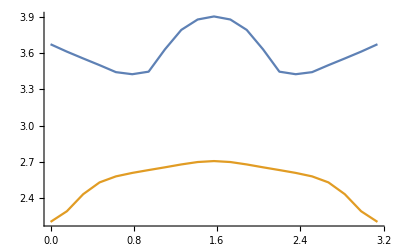

```mathematica
ListLinePlot[{Etmcmax,Etmcmean}]
```

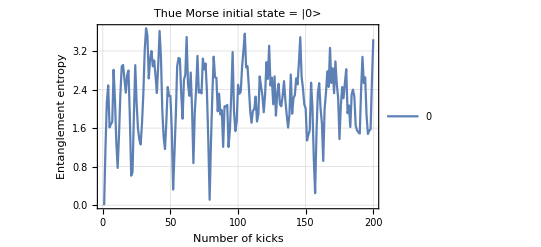

```mathematica
ListLinePlot[Etmcn[[1]],PlotTheme->"Detailed",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotLabel->"Thue Morse initial state = |0>",PlotLegends->{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"}, PlotRange->All]
```

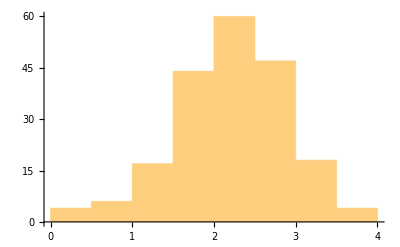
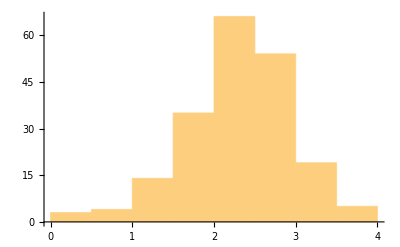
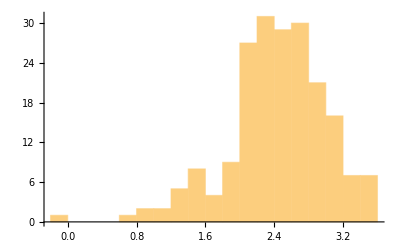
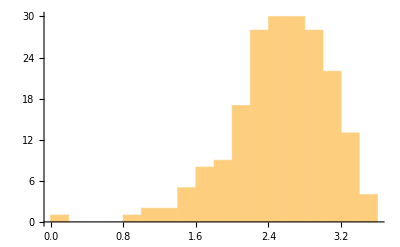
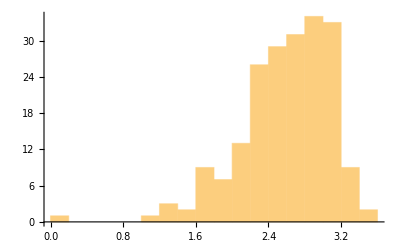
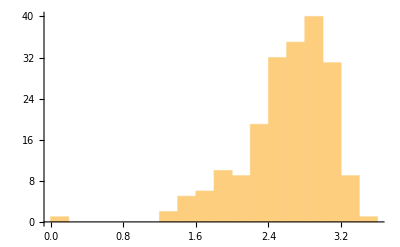
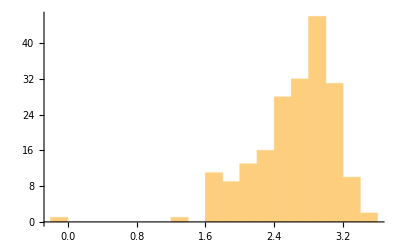
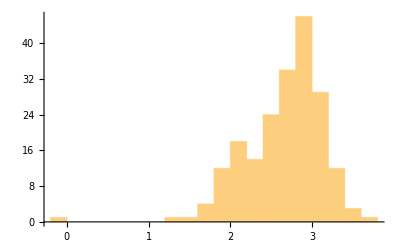

```mathematica
Table[Histogram[Etmcn[[i]]],{i,1,10}]
```

## dt = pi/8

#### data

```mathematica
tm0={-0.000000000000000000*10^+00,6.406853007629834296*10^-16,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.922055902288949598*10^-15,2.562741203051931746*10^-15,1.999999999999999112*10^+00,1.999999999999999112*10^+00,2.562741203051931746*10^-15,3.203426503814914288*10^-15,3.203426503814914288*10^-15,3.844111804577896041*10^-15,1.999999999999998668*10^+00,1.999999999999998224*10^+00,1.999999999999998446*10^+00,1.999999999999998446*10^+00,3.844111804577896041*10^-15,4.484797105340877400*10^-15,4.484797105340877400*10^-15,5.125482406103859548*10^-15,1.999999999999998224*10^+00,1.999999999999998002*10^+00,5.125482406103859548*10^-15,5.766167706866840118*10^-15,1.999999999999997780*10^+00,1.999999999999997780*10^+00,1.999999999999997558*10^+00,1.999999999999997780*10^+00,6.406853007629821477*10^-15,7.047538308392801258*10^-15,1.999999999999997335*10^+00,1.999999999999997335*10^+00,7.367880958774292331*10^-15,8.008566259537272901*10^-15,8.008566259537272901*10^-15,8.649251560300251894*10^-15,1.999999999999996891*10^+00,1.999999999999996447*10^+00,1.089165011297067916*10^-14,1.153233541373365815*10^-14,1.999999999999995559*10^+00,1.999999999999995337*10^+00,1.999999999999995337*10^+00,1.999999999999995337*10^+00,1.601713251907450163*10^-14,1.665781781983747589*10^-14,1.665781781983747589*10^-14,1.729850312060045014*10^-14,1.999999999999993339*10^+00,1.999999999999993339*10^+00,1.999999999999993117*10^+00,1.999999999999993339*10^+00,2.018158697403384220*10^-14,2.082227227479681646*10^-14,1.999999999999991784*10^+00,1.999999999999991784*10^+00,2.146295757555979072*10^-14,2.210364287632276498*10^-14,2.210364287632276498*10^-14,2.274432817708573608*10^-14,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999990896*10^+00,2.306467082746722163*10^-14,2.370535612823019905*10^-14,2.370535612823019905*10^-14,2.434604142899317015*10^-14,1.999999999999990674*10^+00,1.999999999999990674*10^+00,2.402569877861168144*10^-14,2.466638407937465570*10^-14,1.999999999999990674*10^+00,1.999999999999990230*10^+00,1.999999999999990674*10^+00,1.999999999999990230*10^+00,2.498672672975614125*10^-14,2.562741203051911551*10^-14,2.562741203051911551*10^-14,2.626809733128208346*10^-14,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999989564*10^+00,2.690878263204505772*10^-14,2.754946793280802882*10^-14,1.999999999999989342*10^+00,1.999999999999989342*10^+00,2.754946793280802882*10^-14,2.819015323357099993*10^-14,2.819015323357099993*10^-14,2.883083853433397103*10^-14,1.999999999999988898*10^+00,1.999999999999988898*10^+00,3.075289443662288434*10^-14,3.139357973738585544*10^-14,1.999999999999987788*10^+00,1.999999999999987788*10^+00,1.999999999999987788*10^+00,1.999999999999987566*10^+00,3.555803419234514869*10^-14,3.619871949310811348*10^-14,1.999999999999986233*10^+00,1.999999999999986233*10^+00,3.972248864730443562*10^-14,4.036317394806740041*10^-14,4.036317394806740041*10^-14,4.100385924883035889*10^-14,1.999999999999984013*10^+00,1.999999999999984457*10^+00,1.999999999999984235*10^+00,1.999999999999984235*10^+00,4.196488719997481554*10^-14,4.260557250073778034*10^-14,4.260557250073778034*10^-14,4.324625780150074513*10^-14,1.999999999999983569*10^+00,1.999999999999983569*10^+00,4.324625780150074513*10^-14,4.388694310226370361*10^-14,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999983125*10^+00,4.420728575264518285*10^-14,4.484797105340814765*10^-14,1.999999999999982681*10^+00,1.999999999999982681*10^+00,4.452762840302666840*10^-14,4.516831370378963320*10^-14,4.516831370378963320*10^-14,4.580899900455259799*10^-14,1.999999999999982236*10^+00,1.999999999999982236*10^+00,4.548865635417111875*10^-14,4.612934165493407723*10^-14,1.999999999999982236*10^+00,1.999999999999982014*10^+00,1.999999999999982014*10^+00,1.999999999999981792*10^+00,4.709036960607852126*10^-14,4.773105490684148606*10^-14,4.773105490684148606*10^-14,4.837174020760444454*10^-14,1.999999999999981348*10^+00,1.999999999999981348*10^+00,1.999999999999981126*10^+00,1.999999999999981126*10^+00,4.997345345951185337*10^-14,5.061413876027481185*10^-14,1.999999999999980238*10^+00,1.999999999999980460*10^+00,5.381756526408961688*10^-14,5.445825056485256905*10^-14,5.445825056485256905*10^-14,5.509893586561553384*10^-14,1.999999999999978684*10^+00,1.999999999999978684*10^+00,5.862270501981179918*10^-14,5.926339032057475766*10^-14,1.999999999999977129*10^+00,1.999999999999977129*10^+00,1.999999999999976907*10^+00,1.999999999999976907*10^+00,6.150578887324509973*10^-14,6.214647417400807083*10^-14,1.999999999999976019*10^+00,1.999999999999976019*10^+00,6.246681682438955007*10^-14,6.310750212515249593*10^-14,6.310750212515249593*10^-14,6.374818742591545441*10^-14,1.999999999999975575*10^+00,1.999999999999975353*10^+00,1.999999999999975131*10^+00,1.999999999999975131*10^+00,6.406853007629693365*10^-14,6.470921537705987952*10^-14,6.470921537705987952*10^-14,6.534990067782283800*10^-14,1.999999999999974909*10^+00,1.999999999999974909*10^+00,6.502955802744137138*10^-14,6.567024332820431724*10^-14,1.999999999999974687*10^+00,1.999999999999974687*10^+00,1.999999999999974465*10^+00,1.999999999999974243*10^+00,6.599058597858579648*10^-14,6.663127127934874234*10^-14,6.663127127934874234*10^-14,6.727195658011170082*10^-14,1.999999999999974021*10^+00,1.999999999999974021*10^+00,1.999999999999973799*10^+00,1.999999999999974021*10^+00,6.791264188087465930*10^-14,6.855332718163760516*10^-14}
tm005pi={2.722912528242654327*10^-14,2.786981058318951437*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.011220913585990693*10^-14,3.075289443662288434*10^-14,1.929680324037555295*10^+00,1.929680324037555295*10^+00,3.235460768853030579*10^-14,3.299529298929327058*10^-14,3.299529298929327058*10^-14,3.363597829005624800*10^-14,1.929680324037553962*10^+00,1.929680324037553962*10^+00,1.929680324037553962*10^+00,1.929680324037553962*10^+00,3.635889081829885941*10^-14,3.699957611906182420*10^-14,3.699957611906182420*10^-14,3.764026141982478899*10^-14,1.929680324037552630*10^+00,1.929680324037552630*10^+00,4.036317394806740041*10^-14,4.100385924883035889*10^-14,1.929680324037551298*10^+00,1.929680324037551298*10^+00,1.929680324037551298*10^+00,1.929680324037551298*10^+00,4.308608647630999920*10^-14,4.372677177707296399*10^-14,1.929680324037550410*10^+00,1.929680324037550188*10^+00,4.516831370378963320*10^-14,4.612934165493407723*10^-14,4.612934165493407723*10^-14,4.677002695569704202*10^-14,1.929680324037549077*10^+00,1.929680324037549077*10^+00,4.805139755722296530*10^-14,4.869208285798593009*10^-14,1.929680324037548633*10^+00,1.929680324037548633*10^+00,1.929680324037548633*10^+00,1.929680324037548633*10^+00,5.029379610989333261*10^-14,5.093448141065629109*10^-14,5.093448141065629109*10^-14,5.141499538622851626*10^-14,1.929680324037547523*10^+00,1.929680324037547745*10^+00,1.929680324037547523*10^+00,1.929680324037547523*10^+00,5.365739393889887726*10^-14,5.445825056485256905*10^-14,1.929680324037546857*10^+00,1.929680324037546413*10^+00,5.589979249156923194*10^-14,5.654047779233219043*10^-14,5.654047779233219043*10^-14,5.718116309309514260*10^-14,1.929680324037545747*10^+00,1.929680324037545747*10^+00,1.929680324037545525*10^+00,1.929680324037545747*10^+00,5.894304767019327842*10^-14,5.958373297095623690*10^-14,5.958373297095623690*10^-14,6.022441827171919539*10^-14,1.929680324037544414*10^+00,1.929680324037544636*10^+00,6.246681682438955007*10^-14,6.310750212515249593*10^-14,1.929680324037543526*10^+00,1.929680324037543526*10^+00,1.929680324037543304*10^+00,1.929680324037543526*10^+00,6.567024332820431724*10^-14,6.631092862896727572*10^-14,6.631092862896727572*10^-14,6.695161392973023420*10^-14,1.929680324037541972*10^+00,1.929680324037541972*10^+00,1.929680324037541972*10^+00,1.929680324037541972*10^+00,6.935418380759130326*10^-14,6.999486910835424912*10^-14,1.929680324037540862*10^+00,1.929680324037540862*10^+00,7.191692501064311195*10^-14,7.255761031140605781*10^-14,7.255761031140605781*10^-14,7.319829561216901629*10^-14,1.929680324037539751*10^+00,1.929680324037539751*10^+00,7.544069416483933311*10^-14,7.608137946560229159*10^-14,1.929680324037538863*10^+00,1.929680324037538863*10^+00,1.929680324037538419*10^+00,1.929680324037538863*10^+00,7.816360669308186879*10^-14,7.880429199384482728*10^-14,1.929680324037537753*10^+00,1.929680324037537753*10^+00,8.040600524575219824*10^-14,8.104669054651513147*10^-14,8.104669054651513147*10^-14,8.152720452208735034*10^-14,1.929680324037536643*10^+00,1.929680324037537087*10^+00,1.929680324037536643*10^+00,1.929680324037536643*10^+00,8.392977439994839416*10^-14,8.457045970071134002*10^-14,8.457045970071134002*10^-14,8.521114500147428588*10^-14,1.929680324037535311*10^+00,1.929680324037535311*10^+00,8.617217295261871098*10^-14,8.681285825338165684*10^-14,1.929680324037534866*10^+00,1.929680324037534422*10^+00,1.929680324037534866*10^+00,1.929680324037534422*10^+00,8.921542813124270066*10^-14,8.985611343200564652*10^-14,1.929680324037533534*10^+00,1.929680324037533534*10^+00,9.113748403353152562*10^-14,9.193834065948521110*10^-14,9.193834065948521110*10^-14,9.257902596024814433*10^-14,1.929680324037533090*10^+00,1.929680324037532646*10^+00,9.466125318772770891*10^-14,9.514176716329991515*10^-14,1.929680324037531314*10^+00,1.929680324037531758*10^+00,1.929680324037531314*10^+00,1.929680324037531314*10^+00,9.738416571597020673*10^-14,9.802485101673315259*10^-14,9.802485101673315259*10^-14,9.866553631749608583*10^-14,1.929680324037530426*10^+00,1.929680324037530426*10^+00,1.929680324037529981*10^+00,1.929680324037530426*10^+00,1.005875922197848982*10^-13,1.012282775205478440*10^-13,1.929680324037529537*10^+00,1.929680324037529981*10^+00,1.028299907724551897*10^-13,1.034706760732181356*10^-13,1.034706760732181356*10^-13,1.039511900487903418*10^-13,1.929680324037528427*10^+00,1.929680324037528649*10^+00,1.060334172762698812*10^-13,1.066741025770328144*10^-13,1.929680324037527317*10^+00,1.929680324037527761*10^+00,1.929680324037527317*10^+00,1.929680324037527317*10^+00,1.089165011297030934*10^-13,1.095571864304660266*10^-13,1.929680324037526429*10^+00,1.929680324037526429*10^+00,1.114792423327548389*10^-13,1.121199276335177722*10^-13,1.121199276335177722*10^-13,1.127606129342807054*10^-13,1.929680324037525541*10^+00,1.929680324037525097*10^+00,1.929680324037525541*10^+00,1.929680324037525097*10^+00,1.156436967877139050*10^-13,1.164445534136675652*10^-13,1.164445534136675652*10^-13,1.169250673892397715*10^-13,1.929680324037523764*10^+00,1.929680324037523764*10^+00,1.185267806411470667*10^-13,1.191674659419100252*10^-13,1.929680324037522876*10^+00,1.929680324037523098*10^+00,1.929680324037522432*10^+00,1.929680324037522876*10^+00,1.207691791938173457*10^-13,1.215700358197710059*10^-13,1.215700358197710059*10^-13,1.222107211205339391*10^-13,1.929680324037521988*10^+00,1.929680324037521988*10^+00,1.929680324037521766*10^+00,1.929680324037521766*10^+00,1.247734623235856721*10^-13,1.254141476243485801*10^-13}
tm01pi={-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,1.729030204872844978*10^+00,1.729030204872844978*10^+00,1.729030204872844978*10^+00,1.729030204872845200*10^+00,3.203426503814917641*10^-16,1.281370601525966465*10^-15,1.729030204872844756*10^+00,1.729030204872845200*10^+00,2.082227227479694741*10^-15,2.883083853433422820*10^-15,2.722912528242677283*10^-15,3.523769154196404968*10^-15,1.729030204872844312*10^+00,1.729030204872844312*10^+00,1.729030204872844312*10^+00,1.729030204872844312*10^+00,4.324625780150133047*10^-15,4.965311080913113616*10^-15,4.965311080913113616*10^-15,5.766167706866840118*10^-15,1.729030204872843646*10^+00,1.729030204872843646*10^+00,5.926339032057585260*10^-15,6.567024332820566619*10^-15,1.729030204872843868*10^+00,1.729030204872843424*10^+00,1.729030204872843424*10^+00,1.729030204872843424*10^+00,7.848394934346526970*10^-15,8.489080235109505962*10^-15,1.729030204872843202*10^+00,1.729030204872842980*10^+00,1.041113613739844452*10^-14,1.121199276335216944*10^-14,1.121199276335216944*10^-14,1.185267806411514685*10^-14,1.729030204872842091*10^+00,1.729030204872841869*10^+00,1.393490529159482503*10^-14,1.441541926716705493*10^-14,1.729030204872841425*10^+00,1.729030204872840981*10^+00,1.729030204872841647*10^+00,1.729030204872841647*10^+00,1.729850312060045014*10^-14,1.793918842136342756*10^-14,1.793918842136342756*10^-14,1.874004504731714775*10^-14,1.729030204872840315*10^+00,1.729030204872840315*10^+00,1.729030204872839871*10^+00,1.729030204872839871*10^+00,2.098244359998755608*10^-14,2.146295757555979072*10^-14,1.729030204872839205*10^+00,1.729030204872839205*10^+00,2.386552745342093867*10^-14,2.450621275418391293*10^-14,2.466638407937465570*10^-14,2.530706938013762680*10^-14,1.729030204872837873*10^+00,1.729030204872838095*10^+00,1.729030204872837650*10^+00,1.729030204872838095*10^+00,2.674861130685431494*10^-14,2.738929660761728605*10^-14,2.738929660761728605*10^-14,2.786981058318951437*10^-14,1.729030204872837206*10^+00,1.729030204872837206*10^+00,2.899100985952471696*10^-14,2.963169516028768807*10^-14,1.729030204872836762*10^+00,1.729030204872837206*10^+00,1.729030204872836540*10^+00,1.729030204872836762*10^+00,3.219443636333955986*10^-14,3.283512166410253727*10^-14,3.299529298929327058*10^-14,3.347580696486550206*10^-14,1.729030204872835874*10^+00,1.729030204872835874*10^+00,1.729030204872835874*10^+00,1.729030204872835652*10^+00,3.651906214348960534*10^-14,3.715974744425256382*10^-14,1.729030204872834764*10^+00,1.729030204872834986*10^+00,3.892163202135072489*10^-14,3.972248864730443562*10^-14,3.972248864730443562*10^-14,4.020300262287665448*10^-14,1.729030204872833654*10^+00,1.729030204872834098*10^+00,4.196488719997481554*10^-14,4.260557250073778034*10^-14,1.729030204872832988*10^+00,1.729030204872832988*10^+00,1.729030204872832543*10^+00,1.729030204872833210*10^+00,4.452762840302666840*10^-14,4.500814237859889358*10^-14,1.729030204872832321*10^+00,1.729030204872832099*10^+00,4.677002695569704202*10^-14,4.741071225646000051*10^-14,4.741071225646000051*10^-14,4.805139755722296530*10^-14,1.729030204872831433*10^+00,1.729030204872831433*10^+00,1.729030204872831433*10^+00,1.729030204872831433*10^+00,5.013362478470259299*10^-14,5.093448141065629109*10^-14,5.077431008546555147*10^-14,5.141499538622851626*10^-14,1.729030204872830323*10^+00,1.729030204872830323*10^+00,5.301670863813591247*10^-14,5.349722261370813764*10^-14,1.729030204872829657*10^+00,1.729030204872829657*10^+00,1.729030204872829657*10^+00,1.729030204872829435*10^+00,5.638030646714145081*10^-14,5.702099176790440298*10^-14,1.729030204872828769*10^+00,1.729030204872828547*10^+00,5.910321899538401804*10^-14,5.974390429614697652*10^-14,5.974390429614697652*10^-14,6.038458959690993501*10^-14,1.729030204872827658*10^+00,1.729030204872827436*10^+00,6.278715947477102931*10^-14,6.326767345034323555*10^-14,1.729030204872826770*10^+00,1.729030204872826770*10^+00,1.729030204872826326*10^+00,1.729030204872826770*10^+00,6.502955802744137138*10^-14,6.551007200301357762*10^-14,6.551007200301357762*10^-14,6.615075730377653610*10^-14,1.729030204872825660*10^+00,1.729030204872825882*10^+00,1.729030204872825882*10^+00,1.729030204872825438*10^+00,6.743212790530244044*10^-14,6.855332718163760516*10^-14,1.729030204872825216*10^+00,1.729030204872825216*10^+00,7.015504043354500137*10^-14,7.063555440911720761*10^-14,7.063555440911720761*10^-14,7.143641103507089309*10^-14,1.729030204872824328*10^+00,1.729030204872824106*10^+00,7.335846693735974329*10^-14,7.383898091293196215*10^-14,1.729030204872823440*10^+00,1.729030204872823440*10^+00,1.729030204872823440*10^+00,1.729030204872823440*10^+00,7.576103681522081235*10^-14,7.656189344117449783*10^-14,1.729030204872822996*10^+00,1.729030204872822996*10^+00,7.784326404270040217*10^-14,7.864412066865407503*10^-14,7.864412066865407503*10^-14,7.912463464422629389*10^-14,1.729030204872821663*10^+00,1.729030204872821885*10^+00,1.729030204872821663*10^+00,1.729030204872821885*10^+00,8.152720452208735034*10^-14,8.232806114804103582*10^-14,8.232806114804103582*10^-14,8.296874644880398168*10^-14,1.729030204872820775*10^+00,1.729030204872821219*10^+00,8.473063102590209226*10^-14,8.537131632666503812*10^-14,1.729030204872820331*10^+00,1.729030204872820331*10^+00,1.729030204872820331*10^+00,1.729030204872820331*10^+00,8.617217295261871098*10^-14,8.681285825338165684*10^-14,8.681285825338165684*10^-14,8.729337222895387570*10^-14,1.729030204872819665*10^+00,1.729030204872819665*10^+00,1.729030204872819665*10^+00,1.729030204872819221*10^+00,8.921542813124270066*10^-14,8.985611343200564652*10^-14}
tm015pi={9.610279511444749964*10^-16,1.761884577098203667*10^-15,1.427593131110274083*10^+00,1.427593131110274527*10^+00,1.427593131110274083*10^+00,1.427593131110274527*10^+00,4.164454454959387115*10^-15,4.805139755722368474*10^-15,1.427593131110274083*10^+00,1.427593131110274083*10^+00,6.727195658011310973*10^-15,7.528052283965036685*10^-15,7.528052283965036685*10^-15,8.328908909918763186*10^-15,1.427593131110272751*10^+00,1.427593131110272751*10^+00,1.427593131110272973*10^+00,1.427593131110272973*10^+00,9.770450836635465524*10^-15,1.057130746258919045*10^-14,1.057130746258919045*10^-14,1.105182143816142351*10^-14,1.427593131110272751*10^+00,1.427593131110272306*10^+00,1.233319203968737992*10^-14,1.297387734045035891*10^-14,1.427593131110272529*10^+00,1.427593131110272084*10^+00,1.427593131110272306*10^+00,1.427593131110272306*10^+00,1.441541926716705493*10^-14,1.521627589312077828*10^-14,1.427593131110272751*10^+00,1.427593131110272529*10^+00,1.697816047021896459*10^-14,1.793918842136342756*10^-14,1.793918842136342756*10^-14,1.874004504731714775*10^-14,1.427593131110271418*10^+00,1.427593131110271640*10^+00,2.082227227479681646*10^-14,2.146295757555979072*10^-14,1.427593131110270974*10^+00,1.427593131110271418*10^+00,1.427593131110270974*10^+00,1.427593131110270974*10^+00,2.306467082746722163*10^-14,2.354518480303945311*10^-14,2.370535612823019905*10^-14,2.418587010380242737*10^-14,1.427593131110270752*10^+00,1.427593131110270974*10^+00,1.427593131110270752*10^+00,1.427593131110270752*10^+00,2.594775468090060106*10^-14,2.674861130685431494*10^-14,1.427593131110270530*10^+00,1.427593131110270530*10^+00,2.802998190838025715*10^-14,2.851049588395248548*10^-14,2.867066720914323141*10^-14,2.915118118471545658*10^-14,1.427593131110270308*10^+00,1.427593131110270308*10^+00,1.427593131110270308*10^+00,1.427593131110270086*10^+00,3.107323708700436989*10^-14,3.171392238776734100*10^-14,3.187409371295807431*10^-14,3.235460768853030579*10^-14,1.427593131110269642*10^+00,1.427593131110269420*10^+00,3.299529298929327058*10^-14,3.363597829005624800*10^-14,1.427593131110269642*10^+00,1.427593131110269198*10^+00,1.427593131110269642*10^+00,1.427593131110269198*10^+00,3.507752021677292351*10^-14,3.587837684272663424*10^-14,3.587837684272663424*10^-14,3.651906214348960534*10^-14,1.427593131110269198*10^+00,1.427593131110269198*10^+00,1.427593131110269198*10^+00,1.427593131110269198*10^+00,3.844111804577849972*10^-14,3.908180334654146451*10^-14,1.427593131110268976*10^+00,1.427593131110268976*10^+00,4.036317394806740041*10^-14,4.084368792363962558*10^-14,4.084368792363962558*10^-14,4.164454454959332999*10^-14,1.427593131110268310*10^+00,1.427593131110268532*10^+00,4.292591515111925958*10^-14,4.356660045188222437*10^-14,1.427593131110268088*10^+00,1.427593131110268310*10^+00,1.427593131110268088*10^+00,1.427593131110268088*10^+00,4.484797105340814765*10^-14,4.564882767936185206*10^-14,1.427593131110268310*10^+00,1.427593131110267866*10^+00,4.677002695569704202*10^-14,4.741071225646000051*10^-14,4.757088358165074013*10^-14,4.789122623203222568*10^-14,1.427593131110267866*10^+00,1.427593131110267866*10^+00,1.427593131110267866*10^+00,1.427593131110267866*10^+00,4.997345345951185337*10^-14,5.061413876027481185*10^-14,5.077431008546555147*10^-14,5.141499538622851626*10^-14,1.427593131110267421*10^+00,1.427593131110267199*10^+00,5.333705128851739802*10^-14,5.397773658928035019*10^-14,1.427593131110267421*10^+00,1.427593131110266977*10^+00,1.427593131110266977*10^+00,1.427593131110267199*10^+00,5.654047779233219043*10^-14,5.702099176790440298*10^-14,1.427593131110266533*10^+00,1.427593131110266533*10^+00,5.782184839385810108*10^-14,5.862270501981179918*10^-14,5.862270501981179918*10^-14,5.926339032057475766*10^-14,1.427593131110266311*10^+00,1.427593131110266311*10^+00,6.070493224729141425*10^-14,6.118544622286362049*10^-14,1.427593131110265867*10^+00,1.427593131110265645*10^+00,1.427593131110266089*10^+00,1.427593131110265867*10^+00,6.374818742591545441*10^-14,6.422870140148766065*10^-14,6.438887272667840027*10^-14,6.502955802744137138*10^-14,1.427593131110265423*10^+00,1.427593131110265201*10^+00,1.427593131110265645*10^+00,1.427593131110265423*10^+00,6.711178525492097382*10^-14,6.759229923049318006*10^-14,1.427593131110265201*10^+00,1.427593131110264979*10^+00,6.919401248240056364*10^-14,6.951435513278204289*10^-14,6.967452645797276988*10^-14,7.015504043354500137*10^-14,1.427593131110264757*10^+00,1.427593131110264757*10^+00,7.175675368545237233*10^-14,7.207709633583385157*10^-14,1.427593131110265201*10^+00,1.427593131110264757*10^+00,1.427593131110264757*10^+00,1.427593131110264757*10^+00,7.399915223812270177*10^-14,7.463983753888564763*10^-14,1.427593131110264313*10^+00,1.427593131110264313*10^+00,7.640172211598375821*10^-14,7.688223609155597707*10^-14,7.704240741674671669*10^-14,7.784326404270040217*10^-14,1.427593131110264313*10^+00,1.427593131110263869*10^+00,1.427593131110264091*10^+00,1.427593131110264091*10^+00,7.912463464422629389*10^-14,7.976531994498925238*10^-14,7.976531994498925238*10^-14,8.040600524575219824*10^-14,1.427593131110263647*10^+00,1.427593131110263869*10^+00,8.248823247323176282*10^-14,8.312891777399472130*10^-14,1.427593131110262981*10^+00,1.427593131110262981*10^+00,1.427593131110263425*10^+00,1.427593131110262981*10^+00,8.521114500147428588*10^-14,8.601200162742798398*10^-14,8.617217295261871098*10^-14,8.649251560300017760*10^-14,1.427593131110262537*10^+00,1.427593131110262759*10^+00,1.427593131110262537*10^+00,1.427593131110262537*10^+00,8.809422885490754856*10^-14,8.873491415567049442*10^-14}
tm02pi={4.805139755722374982*10^-16,1.281370601525966465*10^-15,1.070009614893122629*10^+00,1.070009614893122407*10^+00,1.070009614893122407*10^+00,1.070009614893122407*10^+00,3.203426503814914288*10^-15,3.844111804577896041*10^-15,1.070009614893122851*10^+00,1.070009614893122851*10^+00,5.605996381676094975*10^-15,6.086510357248330403*10^-15,5.926339032057585260*10^-15,6.567024332820566619*10^-15,1.070009614893123295*10^+00,1.070009614893122629*10^+00,1.070009614893122851*10^+00,1.070009614893122851*10^+00,8.168737584728017255*10^-15,8.969594210681742179*10^-15,8.809422885490996247*10^-15,9.289936861063230886*10^-15,1.070009614893122851*10^+00,1.070009614893123295*10^+00,1.041113613739844452*10^-14,1.121199276335216944*10^-14,1.070009614893123295*10^+00,1.070009614893123295*10^+00,1.070009614893123295*10^+00,1.070009614893123295*10^+00,1.217302071449663556*10^-14,1.281370601525961455*10^-14,1.070009614893123739*10^+00,1.070009614893123961*10^+00,1.393490529159482503*10^-14,1.473576191754854364*10^-14,1.457559059235780087*10^-14,1.521627589312077828*10^-14,1.070009614893124184*10^+00,1.070009614893124628*10^+00,1.665781781983747589*10^-14,1.729850312060045014*10^-14,1.070009614893124850*10^+00,1.070009614893124628*10^+00,1.070009614893124850*10^+00,1.070009614893124628*10^+00,1.922055902288937923*10^-14,1.954090167327086478*10^-14,1.954090167327086478*10^-14,2.002141564884309627*10^-14,1.070009614893125294*10^+00,1.070009614893125294*10^+00,1.070009614893125072*10^+00,1.070009614893124850*10^+00,2.146295757555979072*10^-14,2.178330022594127627*10^-14,1.070009614893125072*10^+00,1.070009614893125072*10^+00,2.274432817708573608*10^-14,2.338501347784871034*10^-14,2.338501347784871034*10^-14,2.354518480303945311*10^-14,1.070009614893126182*10^+00,1.070009614893125960*10^+00,1.070009614893125960*10^+00,1.070009614893126626*10^+00,2.610792600609134068*10^-14,2.674861130685431494*10^-14,2.658843998166357217*10^-14,2.690878263204505772*10^-14,1.070009614893126182*10^+00,1.070009614893126848*10^+00,2.786981058318951437*10^-14,2.835032455876174270*10^-14,1.070009614893127292*10^+00,1.070009614893127292*10^+00,1.070009614893127070*10^+00,1.070009614893127292*10^+00,3.011220913585990693*10^-14,3.059272311143213841*10^-14,3.043255178624139248*10^-14,3.107323708700436989*10^-14,1.070009614893127292*10^+00,1.070009614893127736*10^+00,1.070009614893127514*10^+00,1.070009614893127292*10^+00,3.299529298929327058*10^-14,3.363597829005624800*10^-14,1.070009614893127736*10^+00,1.070009614893127736*10^+00,3.491734889158217758*10^-14,3.555803419234514869*10^-14,3.539786286715440275*10^-14,3.619871949310811348*10^-14,1.070009614893127958*10^+00,1.070009614893128402*10^+00,3.780043274501553493*10^-14,3.812077539539701417*10^-14,1.070009614893128402*10^+00,1.070009614893127958*10^+00,1.070009614893127958*10^+00,1.070009614893128624*10^+00,4.036317394806740041*10^-14,4.068351659844887965*10^-14,1.070009614893129291*10^+00,1.070009614893129068*10^+00,4.196488719997481554*10^-14,4.244540117554703441*10^-14,4.244540117554703441*10^-14,4.324625780150074513*10^-14,1.070009614893129068*10^+00,1.070009614893129513*10^+00,1.070009614893129513*10^+00,1.070009614893129068*10^+00,4.516831370378963320*10^-14,4.580899900455259799*10^-14,4.580899900455259799*10^-14,4.612934165493407723*10^-14,1.070009614893129957*10^+00,1.070009614893129068*10^+00,4.821156888241370492*10^-14,4.869208285798593009*10^-14,1.070009614893129957*10^+00,1.070009614893129513*10^+00,1.070009614893130179*10^+00,1.070009614893130179*10^+00,5.029379610989333261*10^-14,5.061413876027481185*10^-14,1.070009614893129957*10^+00,1.070009614893130401*10^+00,5.173533803660999550*10^-14,5.253619466256369360*10^-14,5.237602333737295398*10^-14,5.301670863813591247*10^-14,1.070009614893130401*10^+00,1.070009614893130179*10^+00,5.445825056485256905*10^-14,5.509893586561553384*10^-14,1.070009614893130401*10^+00,1.070009614893130401*10^+00,1.070009614893130845*10^+00,1.070009614893130401*10^+00,5.670064911752293005*10^-14,5.734133441828588222*10^-14,5.718116309309514260*10^-14,5.782184839385810108*10^-14,1.070009614893130623*10^+00,1.070009614893131067*10^+00,1.070009614893130623*10^+00,1.070009614893130623*10^+00,5.942356164576549728*10^-14,6.006424694652845577*10^-14,1.070009614893131289*10^+00,1.070009614893131289*10^+00,6.150578887324509973*10^-14,6.214647417400807083*10^-14,6.182613152362659159*10^-14,6.262698814958028969*10^-14,1.070009614893131733*10^+00,1.070009614893131955*10^+00,6.342784477553397517*10^-14,6.422870140148766065*10^-14,1.070009614893131733*10^+00,1.070009614893131955*10^+00,1.070009614893131955*10^+00,1.070009614893131955*10^+00,6.534990067782283800*10^-14,6.599058597858579648*10^-14,1.070009614893132177*10^+00,1.070009614893132621*10^+00,6.695161392973023420*10^-14,6.743212790530244044*10^-14,6.743212790530244044*10^-14,6.791264188087465930*10^-14,1.070009614893133287*10^+00,1.070009614893132843*10^+00,1.070009614893133509*10^+00,1.070009614893133065*10^+00,6.983469778316350950*10^-14,7.015504043354500137*10^-14,7.031521175873572837*10^-14,7.063555440911720761*10^-14,1.070009614893133731*10^+00,1.070009614893133287*10^+00,7.223726766102457857*10^-14,7.271778163659681005*10^-14,1.070009614893133731*10^+00,1.070009614893133287*10^+00,1.070009614893133509*10^+00,1.070009614893133287*10^+00,7.447966621369490801*10^-14,7.480000886407638725*10^-14,7.512035151445786649*10^-14,7.560086549003007273*10^-14,1.070009614893134176*10^+00,1.070009614893134398*10^+00,1.070009614893133953*10^+00,1.070009614893134176*10^+00,7.704240741674671669*10^-14,7.752292139231892293*10^-14}
tm025pi={3.203426503814917641*10^-16,3.203426503814917641*10^-16,7.091578053305395146*10^-01,7.091578053305402918*10^-01,7.091578053305399587*10^-01,7.091578053305405138*10^-01,2.562741203051931746*10^-15,3.203426503814914288*10^-15,7.091578053305408469*10^-01,7.091578053305411800*10^-01,4.324625780150133047*10^-15,5.125482406103859548*10^-15,4.805139755722368474*10^-15,5.605996381676094975*10^-15,7.091578053305428453*10^-01,7.091578053305427343*10^-01,7.091578053305434004*10^-01,7.091578053305430673*10^-01,7.207709633583546400*10^-15,8.008566259537272901*10^-15,7.848394934346526970*10^-15,8.649251560300251894*10^-15,7.091578053305436224*10^-01,7.091578053305442886*10^-01,9.450108186253976817*10^-15,9.770450836635465524*10^-15,7.091578053305450657*10^-01,7.091578053305449547*10^-01,7.091578053305457319*10^-01,7.091578053305451768*10^-01,1.153233541373365815*10^-14,1.233319203968737992*10^-14,7.091578053305462870*10^-01,7.091578053305462870*10^-01,1.377473396640408068*10^-14,1.457559059235780087*10^-14,1.441541926716705493*10^-14,1.489593324273928957*10^-14,7.091578053305472862*10^-01,7.091578053305471752*10^-01,1.649764649464672995*10^-14,1.697816047021896459*10^-14,7.091578053305487295*10^-01,7.091578053305480633*10^-01,7.091578053305485074*10^-01,7.091578053305482854*10^-01,1.825953107174491627*10^-14,1.890021637250789053*10^-14,1.890021637250789053*10^-14,1.938073034808011885*10^-14,7.091578053305491736*10^-01,7.091578053305493956*10^-01,7.091578053305493956*10^-01,7.091578053305497287*10^-01,2.050192962441532775*10^-14,2.114261492517830201*10^-14,7.091578053305505058*10^-01,7.091578053305507279*10^-01,2.274432817708573608*10^-14,2.322484215265796756*10^-14,2.322484215265796756*10^-14,2.370535612823019905*10^-14,7.091578053305517271*10^-01,7.091578053305519491*10^-01,7.091578053305517271*10^-01,7.091578053305518381*10^-01,2.594775468090060106*10^-14,2.610792600609134068*10^-14,2.642826865647282939*10^-14,2.674861130685431494*10^-14,7.091578053305532814*10^-01,7.091578053305531704*10^-01,2.819015323357099993*10^-14,2.867066720914323141*10^-14,7.091578053305542806*10^-01,7.091578053305538365*10^-01,7.091578053305547247*10^-01,7.091578053305541696*10^-01,3.075289443662288434*10^-14,3.123340841219510951*10^-14,3.107323708700436989*10^-14,3.155375106257659506*10^-14,7.091578053305555018*10^-01,7.091578053305551688*10^-01,7.091578053305553908*10^-01,7.091578053305552798*10^-01,3.331563563967475613*10^-14,3.395632094043772724*10^-14,7.091578053305561680*10^-01,7.091578053305559459*10^-01,3.507752021677292351*10^-14,3.555803419234514869*10^-14,3.555803419234514869*10^-14,3.619871949310811348*10^-14,7.091578053305580553*10^-01,7.091578053305572782*10^-01,3.780043274501553493*10^-14,3.844111804577849972*10^-14,7.091578053305582774*10^-01,7.091578053305584994*10^-01,7.091578053305584994*10^-01,7.091578053305586105*10^-01,4.004283129768591486*10^-14,4.036317394806740041*10^-14,7.091578053305596097*10^-01,7.091578053305592766*10^-01,4.196488719997481554*10^-14,4.260557250073778034*10^-14,4.260557250073778034*10^-14,4.292591515111925958*10^-14,7.091578053305610529*10^-01,7.091578053305609419*10^-01,7.091578053305606089*10^-01,7.091578053305610529*10^-01,4.500814237859889358*10^-14,4.564882767936185206*10^-14,4.548865635417111875*10^-14,4.580899900455259799*10^-14,7.091578053305619411*10^-01,7.091578053305622742*10^-01,4.741071225646000051*10^-14,4.805139755722296530*10^-14,7.091578053305632734*10^-01,7.091578053305631624*10^-01,7.091578053305634954*10^-01,7.091578053305640505*10^-01,4.965311080913036781*10^-14,4.997345345951185337*10^-14,7.091578053305647167*10^-01,7.091578053305641616*10^-01,5.125482406103777033*10^-14,5.205568068699146843*10^-14,5.189550936180072881*10^-14,5.253619466256369360*10^-14,7.091578053305659379*10^-01,7.091578053305662710*10^-01,5.413790791447108981*10^-14,5.477859321523404829*10^-14,7.091578053305670482*10^-01,7.091578053305669371*10^-01,7.091578053305670482*10^-01,7.091578053305668261*10^-01,5.605996381675997156*10^-14,5.686082044271366336*10^-14,5.686082044271366336*10^-14,5.750150574347662184*10^-14,7.091578053305681584*10^-01,7.091578053305682694*10^-01,7.091578053305681584*10^-01,7.091578053305684914*10^-01,5.974390429614697652*10^-14,6.022441827171919539*10^-14,7.091578053305692686*10^-01,7.091578053305694906*10^-01,6.182613152362659159*10^-14,6.230664549919881045*10^-14,6.246681682438955007*10^-14,6.294733079996175631*10^-14,7.091578053305712670*10^-01,7.091578053305707119*10^-01,6.438887272667840027*10^-14,6.454904405186913989*10^-14,7.091578053305713780*10^-01,7.091578053305719331*10^-01,7.091578053305717111*10^-01,7.091578053305720442*10^-01,6.631092862896727572*10^-14,6.663127127934874234*10^-14,7.091578053305725993*10^-01,7.091578053305722662*10^-01,6.823298453125612592*10^-14,6.855332718163760516*10^-14,6.855332718163760516*10^-14,6.903384115720982402*10^-14,7.091578053305734874*10^-01,7.091578053305737095*10^-01,7.091578053305739315*10^-01,7.091578053305735985*10^-01,7.079572573430794723*10^-14,7.127623970988015347*10^-14,7.127623970988015347*10^-14,7.159658236026163271*10^-14,7.091578053305751528*10^-01,7.091578053305750418*10^-01,7.303812428697827667*10^-14,7.367880958774122253*10^-14,7.091578053305764850*10^-01,7.091578053305760410*10^-01,7.091578053305769291*10^-01,7.091578053305761520*10^-01,7.544069416483933311*10^-14,7.624155079079303121*10^-14,7.624155079079303121*10^-14,7.656189344117449783*10^-14,7.091578053305775953*10^-01,7.091578053305782614*10^-01,7.091578053305777063*10^-01,7.091578053305783724*10^-01,7.864412066865407503*10^-14,7.912463464422629389*10^-14}
tm03pi={-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,3.871470010700654996*10^-01,3.871470010700654441*10^-01,3.871470010700660547*10^-01,3.871470010700656661*10^-01,1.601713251907457933*10^-15,2.562741203051931746*10^-15,3.871470010700672759*10^-01,3.871470010700674980*10^-01,4.164454454959387115*10^-15,4.805139755722368474*10^-15,4.805139755722368474*10^-15,5.125482406103859548*10^-15,3.871470010700689413*10^-01,3.871470010700694964*10^-01,3.871470010700695519*10^-01,3.871470010700699405*10^-01,7.367880958774292331*10^-15,7.688223609155782616*10^-15,8.008566259537272901*10^-15,8.328908909918763186*10^-15,3.871470010700718278*10^-01,3.871470010700724385*10^-01,9.930622161826211456*10^-15,1.041113613739844452*10^-14,3.871470010700737152*10^-01,3.871470010700741593*10^-01,3.871470010700741593*10^-01,3.871470010700743813*10^-01,1.313404866564110168*10^-14,1.345439131602259039*10^-14,3.871470010700763797*10^-01,3.871470010700761022*10^-01,1.537644721831152421*10^-14,1.601713251907450163*10^-14,1.601713251907450163*10^-14,1.633747516945598718*10^-14,3.871470010700779896*10^-01,3.871470010700783781*10^-01,1.825953107174491627*10^-14,1.825953107174491627*10^-14,3.871470010700794884*10^-01,3.871470010700791553*10^-01,3.871470010700802100*10^-01,3.871470010700797104*10^-01,2.098244359998755608*10^-14,2.146295757555979072*10^-14,2.146295757555979072*10^-14,2.210364287632276498*10^-14,3.871470010700825970*10^-01,3.871470010700820419*10^-01,3.871470010700825970*10^-01,3.871470010700827080*10^-01,2.402569877861168144*10^-14,2.450621275418391293*10^-14,3.871470010700839293*10^-01,3.871470010700837627*10^-01,2.626809733128208346*10^-14,2.690878263204505772*10^-14,2.722912528242654327*10^-14,2.738929660761728605*10^-14,3.871470010700865938*10^-01,3.871470010700870934*10^-01,3.871470010700866493*10^-01,3.871470010700869824*10^-01,2.947152383509694213*10^-14,2.979186648547842769*10^-14,3.011220913585990693*10^-14,3.027238046105065286*10^-14,3.871470010700888698*10^-01,3.871470010700888142*10^-01,3.203426503814882024*10^-14,3.267495033891179134*10^-14,3.871470010700909237*10^-01,3.871470010700911457*10^-01,3.871470010700910902*10^-01,3.871470010700914233*10^-01,3.459700624120069834*10^-14,3.523769154196366944*10^-14,3.523769154196366944*10^-14,3.587837684272663424*10^-14,3.871470010700930331*10^-01,3.871470010700928666*10^-01,3.871470010700935327*10^-01,3.871470010700930331*10^-01,3.812077539539701417*10^-14,3.844111804577849972*10^-14,3.871470010700950315*10^-01,3.871470010700948094*10^-01,4.020300262287665448*10^-14,4.036317394806740041*10^-14,4.068351659844887965*10^-14,4.100385924883035889*10^-14,3.871470010700967523*10^-01,3.871470010700971409*10^-01,4.324625780150074513*10^-14,4.356660045188222437*10^-14,3.871470010700992503*10^-01,3.871470010700986397*10^-01,3.871470010700989728*10^-01,3.871470010700988063*10^-01,4.548865635417111875*10^-14,4.644968430531555647*10^-14,3.871470010701011377*10^-01,3.871470010701002495*10^-01,4.805139755722296530*10^-14,4.837174020760444454*10^-14,4.869208285798593009*10^-14,4.901242550836740933*10^-14,3.871470010701030806*10^-01,3.871470010701031916*10^-01,3.871470010701035802*10^-01,3.871470010701032471*10^-01,5.109465273584703071*10^-14,5.157516671141925588*10^-14,5.189550936180072881*10^-14,5.253619466256369360*10^-14,3.871470010701048015*10^-01,3.871470010701051345*10^-01,5.397773658928035019*10^-14,5.445825056485256905*10^-14,3.871470010701065778*10^-01,3.871470010701067999*10^-01,3.871470010701070774*10^-01,3.871470010701072995*10^-01,5.638030646714145081*10^-14,5.670064911752293005*10^-14,3.871470010701089648*10^-01,3.871470010701092423*10^-01,5.894304767019327842*10^-14,5.894304767019327842*10^-14,5.926339032057475766*10^-14,5.990407562133771614*10^-14,3.871470010701112408*10^-01,3.871470010701112963*10^-01,6.134561754805436011*10^-14,6.230664549919881045*10^-14,3.871470010701133502*10^-01,3.871470010701136832*10^-01,3.871470010701134057*10^-01,3.871470010701136832*10^-01,6.422870140148766065*10^-14,6.502955802744137138*10^-14,6.454904405186913989*10^-14,6.567024332820431724*10^-14,3.871470010701158482*10^-01,3.871470010701154596*10^-01,3.871470010701159037*10^-01,3.871470010701159037*10^-01,6.727195658011170082*10^-14,6.823298453125612592*10^-14,3.871470010701172360*10^-01,3.871470010701176800*10^-01,6.983469778316350950*10^-14,7.015504043354500137*10^-14,7.015504043354500137*10^-14,7.079572573430794723*10^-14,3.871470010701196784*10^-01,3.871470010701190123*10^-01,7.239743898621531819*10^-14,7.271778163659681005*10^-14,3.871470010701215103*10^-01,3.871470010701215103*10^-01,3.871470010701217879*10^-01,3.871470010701215658*10^-01,7.480000886407638725*10^-14,7.544069416483933311*10^-14,3.871470010701233422*10^-01,3.871470010701231756*10^-01,7.736275006712818331*10^-14,7.720257874193745631*10^-14,7.752292139231892293*10^-14,7.816360669308186879*10^-14,3.871470010701260622*10^-01,3.871470010701261177*10^-01,3.871470010701261732*10^-01,3.871470010701264508*10^-01,8.056617657094293786*10^-14,8.072634789613366486*10^-14,8.072634789613366486*10^-14,8.136703319689661072*10^-14,3.871470010701277831*10^-01,3.871470010701280051*10^-01,8.328908909918546092*10^-14,8.392977439994839416*10^-14,3.871470010701302256*10^-01,3.871470010701298370*10^-01,3.871470010701303366*10^-01,3.871470010701301145*10^-01,8.617217295261871098*10^-14,8.665268692819092984*10^-14,8.649251560300017760*10^-14,8.713320090376312346*10^-14,3.871470010701317799*10^-01,3.871470010701314468*10^-01,3.871470010701318354*10^-01,3.871470010701315578*10^-01,8.873491415567049442*10^-14,8.937559945643342766*10^-14}
tm035pi={-3.203426503814917641*10^-16,1.601713251907458574*10^-16,1.697508061995215145*10^-01,1.697508061995220974*10^-01,1.697508061995220974*10^-01,1.697508061995222362*10^-01,2.722912528242677283*10^-15,2.722912528242677283*10^-15,1.697508061995253170*10^-01,1.697508061995249284*10^-01,5.766167706866840118*10^-15,6.086510357248330403*10^-15,6.086510357248330403*10^-15,6.727195658011310973*10^-15,1.697508061995276207*10^-01,1.697508061995279538*10^-01,1.697508061995281481*10^-01,1.697508061995285367*10^-01,9.129765535872486532*10^-15,9.610279511444719593*10^-15,9.930622161826211456*10^-15,1.025096481220770016*10^-14,1.697508061995317563*10^-01,1.697508061995313122*10^-01,1.249336336487812427*10^-14,1.281370601525961455*10^-14,1.697508061995344764*10^-01,1.697508061995337547*10^-01,1.697508061995346706*10^-01,1.697508061995345596*10^-01,1.537644721831152421*10^-14,1.585696119388375570*10^-14,1.697508061995378625*10^-01,1.697508061995382234*10^-01,1.825953107174491627*10^-14,1.890021637250789053*10^-14,1.890021637250789053*10^-14,1.954090167327086478*10^-14,1.697508061995400830*10^-01,1.697508061995408324*10^-01,2.146295757555979072*10^-14,2.210364287632276498*10^-14,1.697508061995436357*10^-01,1.697508061995430251*10^-01,1.697508061995428030*10^-01,1.697508061995427753*10^-01,2.466638407937465570*10^-14,2.530706938013762680*10^-14,2.530706938013762680*10^-14,2.546724070532837274*10^-14,1.697508061995463557*10^-01,1.697508061995467443*10^-01,1.697508061995461059*10^-01,1.697508061995465778*10^-01,2.883083853433397103*10^-14,2.883083853433397103*10^-14,1.697508061995487427*10^-01,1.697508061995486317*10^-01,3.139357973738585544*10^-14,3.171392238776734100*10^-14,3.203426503814882024*10^-14,3.219443636333955986*10^-14,1.697508061995526285*10^-01,1.697508061995521567*10^-01,1.697508061995528506*10^-01,1.697508061995524342*10^-01,3.491734889158217758*10^-14,3.587837684272663424*10^-14,3.555803419234514869*10^-14,3.587837684272663424*10^-14,1.697508061995552098*10^-01,1.697508061995551543*10^-01,3.780043274501553493*10^-14,3.844111804577849972*10^-14,1.697508061995585127*10^-01,1.697508061995582074*10^-01,1.697508061995591511*10^-01,1.697508061995588735*10^-01,4.164454454959332999*10^-14,4.196488719997481554*10^-14,4.180471587478406961*10^-14,4.260557250073778034*10^-14,1.697508061995615380*10^-01,1.697508061995616213*10^-01,1.697508061995619544*10^-01,1.697508061995620099*10^-01,4.484797105340814765*10^-14,4.532848502898037282*10^-14,1.697508061995644524*10^-01,1.697508061995640360*10^-01,4.805139755722296530*10^-14,4.837174020760444454*10^-14,4.837174020760444454*10^-14,4.885225418317666971*10^-14,1.697508061995668949*10^-01,1.697508061995681716*10^-01,5.093448141065629109*10^-14,5.157516671141925588*10^-14,1.697508061995700313*10^-01,1.697508061995696149*10^-01,1.697508061995697259*10^-01,1.697508061995699202*10^-01,5.413790791447108981*10^-14,5.445825056485256905*10^-14,1.697508061995726958*10^-01,1.697508061995729178*10^-01,5.638030646714145081*10^-14,5.734133441828588222*10^-14,5.702099176790440298*10^-14,5.814219104423958032*10^-14,1.697508061995755546*10^-01,1.697508061995752493*10^-01,1.697508061995757767*10^-01,1.697508061995754713*10^-01,6.054476092210067463*10^-14,6.118544622286362049*10^-14,6.086510357248215387*10^-14,6.150578887324509973*10^-14,1.697508061995790241*10^-01,1.697508061995789963*10^-01,6.438887272667840027*10^-14,6.406853007629693365*10^-14,1.697508061995817719*10^-01,1.697508061995827155*10^-01,1.697508061995816608*10^-01,1.697508061995825768*10^-01,6.727195658011170082*10^-14,6.759229923049318006*10^-14,1.697508061995845752*10^-01,1.697508061995842976*10^-01,6.983469778316350950*10^-14,7.079572573430794723*10^-14,7.047538308392646799*10^-14,7.095589705949868685*10^-14,1.697508061995887663*10^-01,1.697508061995889328*10^-01,7.367880958774122253*10^-14,7.399915223812270177*10^-14,1.697508061995909312*10^-01,1.697508061995902651*10^-01,1.697508061995910700*10^-01,1.697508061995909034*10^-01,7.624155079079303121*10^-14,7.656189344117449783*10^-14,7.672206476636523745*10^-14,7.720257874193745631*10^-14,1.697508061995942619*10^-01,1.697508061995942064*10^-01,1.697508061995940121*10^-01,1.697508061995939566*10^-01,7.976531994498925238*10^-14,7.976531994498925238*10^-14,1.697508061995974260*10^-01,1.697508061995967599*10^-01,8.248823247323176282*10^-14,8.328908909918546092*10^-14,8.360943174956692754*10^-14,8.392977439994839416*10^-14,1.697508061996005624*10^-01,1.697508061995999518*10^-01,8.617217295261871098*10^-14,8.681285825338165684*10^-14,1.697508061996023110*10^-01,1.697508061996028383*10^-01,1.697508061996025053*10^-01,1.697508061996031714*10^-01,8.969594210681490690*10^-14,9.001628475719637352*10^-14,1.697508061996052808*10^-01,1.697508061996056139*10^-01,9.257902596024814433*10^-14,9.289936861062962357*10^-14,9.289936861062962357*10^-14,9.337988258620182981*10^-14,1.697508061996085837*10^-01,1.697508061996090278*10^-01,1.697508061996090833*10^-01,1.697508061996093609*10^-01,9.610279511444432763*10^-14,9.674348041520727349*10^-14,9.674348041520727349*10^-14,9.706382306558874011*10^-14,1.697508061996121365*10^-01,1.697508061996121365*10^-01,9.930622161825901907*10^-14,1.001070782442127045*10^-13,1.697508061996154116*10^-01,1.697508061996160222*10^-01,1.697508061996157169*10^-01,1.697508061996155782*10^-01,1.025096481220737231*10^-13,1.033105047480273960*10^-13,1.036308473984088626*10^-13,1.037910187235995896*10^-13,1.697508061996183260*10^-01,1.697508061996176876*10^-01,1.697508061996186868*10^-01,1.697508061996181594*10^-01,1.063537599266513478*10^-13,1.066741025770328144*10^-13}
tm04pi={-3.203426503814917641*10^-16,3.203426503814917641*10^-16,4.658712630365312302*10^-02,4.658712630365402507*10^-02,4.658712630365374058*10^-02,4.658712630365390017*10^-02,3.203426503814914288*10^-15,3.683940479387150899*10^-15,4.658712630365741819*10^-02,4.658712630365721696*10^-02,6.567024332820566619*10^-15,6.887366983202056115*10^-15,7.688223609155782616*10^-15,7.367880958774292331*10^-15,4.658712630366049212*10^-02,4.658712630366087376*10^-02,4.658712630366142193*10^-02,4.658712630366142887*10^-02,1.073147878777993322*10^-14,1.137216408854291222*10^-14,1.137216408854291222*10^-14,1.185267806411514685*10^-14,4.658712630366592528*10^-02,4.658712630366577262*10^-02,1.473576191754854364*10^-14,1.505610456793003235*10^-14,4.658712630366840940*10^-02,4.658712630366821511*10^-02,4.658712630366934615*10^-02,4.658712630366881186*10^-02,1.874004504731714775*10^-14,1.922055902288937923*10^-14,4.658712630367212865*10^-02,4.658712630367251722*10^-02,2.194347155113201904*10^-14,2.226381420151350460*10^-14,2.290449950227647886*10^-14,2.290449950227647886*10^-14,4.658712630367711077*10^-02,4.658712630367566748*10^-02,2.578758335570985829*10^-14,2.642826865647282939*10^-14,4.658712630367856100*10^-02,4.658712630367894958*10^-02,4.658712630367928959*10^-02,4.658712630367903978*10^-02,2.963169516028768807*10^-14,3.027238046105065286*10^-14,3.011220913585990693*10^-14,3.075289443662288434*10^-14,4.658712630368262025*10^-02,4.658712630368291863*10^-02,4.658712630368331414*10^-02,4.658712630368290475*10^-02,3.283512166410253727*10^-14,3.427666359081921279*10^-14,4.658712630368676971*10^-02,4.658712630368601337*10^-02,3.715974744425256382*10^-14,3.780043274501553493*10^-14,3.780043274501553493*10^-14,3.844111804577849972*10^-14,4.658712630369099550*10^-02,4.658712630369127305*10^-02,4.658712630369055835*10^-02,4.658712630369126612*10^-02,4.148437322440259037*10^-14,4.164454454959332999*10^-14,4.132420189921184444*10^-14,4.228522985035629479*10^-14,4.658712630369511720*10^-02,4.658712630369524210*10^-02,4.516831370378963320*10^-14,4.580899900455259799*10^-14,4.658712630369919727*10^-02,4.658712630369901686*10^-02,4.658712630369935687*10^-02,4.658712630369947483*10^-02,4.917259683355814264*10^-14,4.965311080913036781*10^-14,4.933276815874888857*10^-14,4.997345345951185337*10^-14,4.658712630370291652*10^-02,4.658712630370277774*10^-02,4.658712630370261121*10^-02,4.658712630370321489*10^-02,5.301670863813591247*10^-14,5.381756526408961688*10^-14,4.658712630370614310*10^-02,4.658712630370617780*10^-02,5.638030646714145081*10^-14,5.718116309309514260*10^-14,5.670064911752293005*10^-14,5.750150574347662184*10^-14,4.658712630370995950*10^-02,4.658712630371087543*10^-02,6.022441827171919539*10^-14,6.086510357248215387*10^-14,4.658712630371333874*10^-02,4.658712630371295016*10^-02,4.658712630371381058*10^-02,4.658712630371312363*10^-02,6.470921537705987952*10^-14,6.502955802744137138*10^-14,4.658712630371706492*10^-02,4.658712630371780739*10^-02,6.759229923049318006*10^-14,6.823298453125612592*10^-14,6.759229923049318006*10^-14,6.855332718163760516*10^-14,4.658712630372122826*10^-02,4.658712630372017355*10^-02,4.658712630372077029*10^-02,4.658712630372040947*10^-02,7.207709633583385157*10^-14,7.223726766102457857*10^-14,7.223726766102457857*10^-14,7.271778163659681005*10^-14,4.658712630372442709*10^-02,4.658712630372490587*10^-02,7.528052283964860611*10^-14,7.576103681522081235*10^-14,4.658712630372766061*10^-02,4.658712630372797980*10^-02,4.658712630372878472*10^-02,4.658712630372839614*10^-02,7.912463464422629389*10^-14,7.976531994498925238*10^-14,4.658712630373144231*10^-02,4.658712630373158109*10^-02,8.296874644880398168*10^-14,8.328908909918546092*10^-14,8.360943174956692754*10^-14,8.392977439994839416*10^-14,4.658712630373615382*10^-02,4.658712630373565422*10^-02,8.681285825338165684*10^-14,8.745354355414460270*10^-14,4.658712630373913061*10^-02,4.658712630373899183*10^-02,4.658712630373932490*10^-02,4.658712630373863101*10^-02,9.033662740757785276*10^-14,9.049679873276857976*10^-14,9.129765535872226524*10^-14,9.113748403353152562*10^-14,4.658712630374289149*10^-02,4.658712630374381436*10^-02,4.658712630374322455*10^-02,4.658712630374334251*10^-02,9.498159583810918815*10^-14,9.514176716329991515*10^-14,4.658712630374683972*10^-02,4.658712630374701319*10^-02,9.834519366711461921*10^-14,9.962656426864049831*10^-14,9.898587896787756507*10^-14,9.930622161825901907*10^-14,4.658712630375042019*10^-02,4.658712630375100305*10^-02,1.023494767968829961*10^-13,1.028299907724551897*10^-13,4.658712630375427127*10^-02,4.658712630375420188*10^-02,4.658712630375477087*10^-02,4.658712630375527741*10^-02,1.058732459510791416*10^-13,1.073147878777957603*10^-13,4.658712630375796970*10^-02,4.658712630375744235*10^-02,1.092368437800845600*10^-13,1.093970151052752996*10^-13,1.098775290808474932*10^-13,1.101978717312289598*10^-13,4.658712630376137670*10^-02,4.658712630376167507*10^-02,4.658712630376157099*10^-02,4.658712630376227182*10^-02,1.134012982350436260*10^-13,1.142021548609972863*10^-13,1.140419835358065593*10^-13,1.148428401617602195*10^-13,4.658712630376573433*10^-02,4.658712630376563718*10^-02,1.178860953403841335*10^-13,1.178860953403841335*10^-13,4.658712630376963398*10^-02,4.658712630376964786*10^-02,4.658712630376980746*10^-02,4.658712630376984215*10^-02,1.214098644945802537*10^-13,1.222107211205339391*10^-13,1.222107211205339391*10^-13,1.222107211205339391*10^-13,4.658712630377426223*10^-02,4.658712630377405406*10^-02,4.658712630377431774*10^-02,4.658712630377433855*10^-02,1.262150042503022403*10^-13,1.258946615999207863*10^-13}
tm045pi={-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,4.319582673447943874*10^-04,4.319582673441538950*10^-04,4.319582673444741141*10^-04,4.319582673449545241*10^-04,4.324625780150133047*10^-15,3.683940479387150899*10^-15,4.319582673483171229*10^-04,4.319582673495981078*10^-04,8.328908909918763186*10^-15,8.649251560300251894*10^-15,8.328908909918763186*10^-15,9.770450836635465524*10^-15,4.319582673529606524*10^-04,4.319582673531207890*10^-04,4.319582673536011448*10^-04,4.319582673536011448*10^-04,1.265353469006887020*10^-14,1.313404866564110168*10^-14,1.313404866564110168*10^-14,1.361456264121333632*10^-14,4.319582673588852209*10^-04,4.319582673584048652*10^-04,1.761884577098193885*10^-14,1.777901709617268478*10^-14,4.319582673614472449*10^-04,4.319582673616073273*10^-04,4.319582673622478198*10^-04,4.319582673616073273*10^-04,2.178330022594127627*10^-14,2.242398552670425053*10^-14,4.319582673660907744*10^-04,4.319582673659306377*10^-04,2.562741203051911551*10^-14,2.546724070532837274*10^-14,2.562741203051911551*10^-14,2.610792600609134068*10^-14,4.319582673702539481*10^-04,4.319582673702539481*10^-04,3.043255178624139248*10^-14,3.075289443662288434*10^-14,4.319582673748975860*10^-04,4.319582673745773127*10^-04,4.319582673742570936*10^-04,4.319582673747374493*10^-04,3.459700624120069834*10^-14,3.491734889158217758*10^-14,3.507752021677292351*10^-14,3.491734889158217758*10^-14,4.319582673792208964*10^-04,4.319582673790607597*10^-04,4.319582673800214712*10^-04,4.319582673785804039*10^-04,3.876146069615998527*10^-14,3.988265997249516892*10^-14,4.319582673833840701*10^-04,4.319582673838644801*10^-04,4.244540117554703441*10^-14,4.388694310226370361*10^-14,4.372677177707296399*10^-14,4.372677177707296399*10^-14,4.319582673881877904*10^-04,4.319582673885080095*10^-04,4.319582673881877904*10^-04,4.319582673885080095*10^-04,4.741071225646000051*10^-14,4.821156888241370492*10^-14,4.853191153279518416*10^-14,4.869208285798593009*10^-14,4.319582673925111008*10^-04,4.319582673928313741*10^-04,5.157516671141925588*10^-14,5.237602333737295398*10^-14,4.319582673965141921*10^-04,4.319582673966743287*10^-04,4.319582673965141921*10^-04,4.319582673968344112*10^-04,5.654047779233219043*10^-14,5.702099176790440298*10^-14,5.702099176790440298*10^-14,5.750150574347662184*10^-14,4.319582674013179124*10^-04,4.319582674008375566*10^-04,4.319582674017983224*10^-04,4.319582674016381315*10^-04,6.118544622286362049*10^-14,6.150578887324509973*10^-14,4.319582674051608670*10^-04,4.319582674054811403*10^-04,6.502955802744137138*10^-14,6.534990067782283800*10^-14,6.502955802744137138*10^-14,6.599058597858579648*10^-14,4.319582674099645332*10^-04,4.319582674102848607*10^-04,6.919401248240056364*10^-14,7.015504043354500137*10^-14,4.319582674139676786*10^-04,4.319582674141277611*10^-04,4.319582674146081711*10^-04,4.319582674146081711*10^-04,7.399915223812270177*10^-14,7.415932356331344139*10^-14,4.319582674190915639*10^-04,4.319582674187713448*10^-04,7.752292139231892293*10^-14,7.816360669308186879*10^-14,7.816360669308186879*10^-14,7.848394934346334803*10^-14,4.319582674226142994*10^-04,4.319582674222940803*10^-04,4.319582674232547918*10^-04,4.319582674229345727*10^-04,8.312891777399472130*10^-14,8.344926042437620054*10^-14,8.360943174956692754*10^-14,8.344926042437620054*10^-14,4.319582674269376640*10^-04,4.319582674278983755*10^-04,8.761371487933532970*10^-14,8.809422885490754856*10^-14,4.319582674323818768*10^-04,4.319582674314211110*10^-04,4.319582674322216859*10^-04,4.319582674319014668*10^-04,9.145782668391300486*10^-14,9.177816933429447148*10^-14,4.319582674367051871*10^-04,4.319582674363849138*10^-04,9.578245246406286101*10^-14,9.610279511444432763*10^-14,9.594262378925358801*10^-14,9.658330909001653387*10^-14,4.319582674405481417*10^-04,4.319582674411886342*10^-04,9.962656426864049831*10^-14,1.001070782442127045*10^-13,4.319582674442310139*10^-04,4.319582674445512330*10^-04,4.319582674440708230*10^-04,4.319582674437506039*10^-04,1.036308473984088626*10^-13,1.041113613739810688*10^-13,1.037910187235995896*10^-13,1.047520466747440021*10^-13,4.319582674491948167*10^-04,4.319582674490346258*10^-04,4.319582674496751725*10^-04,4.319582674496751725*10^-04,1.084359871541308871*10^-13,1.085961584793216141*10^-13,4.319582674531978537*10^-04,4.319582674528776346*10^-04,1.129207842594714324*10^-13,1.127606129342807054*10^-13,1.127606129342807054*10^-13,1.138818122106158323*10^-13,4.319582674573610817*10^-04,4.319582674567205892*10^-04,1.169250673892397715*10^-13,1.169250673892397715*10^-13,4.319582674608837629*10^-04,4.319582674610439538*10^-04,4.319582674612040363*10^-04,4.319582674607236805*10^-04,1.212496931693895267*10^-13,1.217302071449617329*10^-13,4.319582674652071275*10^-04,4.319582674648868542*10^-04,1.249336336487763738*10^-13,1.258946615999207863*10^-13,1.255743189495393071*10^-13,1.263751755754929673*10^-13,4.319582674696905746*10^-04,4.319582674696905746*10^-04,4.319582674700108479*10^-04,4.319582674701709845*10^-04,1.300591160548798145*10^-13,1.300591160548798145*10^-13,1.302192873800705163*10^-13,1.303794587052612433*10^-13,4.319582674751347873*10^-04,4.319582674748145140*10^-04,1.343837418350295444*10^-13,1.343837418350295444*10^-13,4.319582674789777419*10^-04,4.319582674781771128*10^-04,4.319582674791378786*10^-04,4.319582674788176053*10^-04,1.379075109892256141*10^-13,1.387083676151792744*10^-13,1.383880249647977951*10^-13,1.388685389403699761*10^-13,4.319582674831409157*10^-04,4.319582674829808332*10^-04,4.319582674839415990*10^-04,4.319582674839415990*10^-04,1.425524794197567981*10^-13,1.430329933953289791*10^-13}
tm05pi={-0.000000000000000000*10^+00,6.406853007629834296*10^-16,2.242398552670440672*10^-15,1.281370601525966465*10^-15,2.402569877861186209*10^-15,2.242398552670440672*10^-15,3.683940479387150899*10^-15,4.164454454959387115*10^-15,6.406853007629821477*10^-15,7.207709633583546400*10^-15,8.008566259537272901*10^-15,8.008566259537272901*10^-15,8.328908909918763186*10^-15,8.969594210681742179*10^-15,1.073147878777993322*10^-14,1.073147878777993322*10^-14,1.169250673892440250*10^-14,1.169250673892440250*10^-14,1.297387734045035891*10^-14,1.329421999083184604*10^-14,1.329421999083184604*10^-14,1.409507661678556938*10^-14,1.505610456793003235*10^-14,1.553661854350226699*10^-14,1.729850312060045014*10^-14,1.745867444579119608*10^-14,1.938073034808011885*10^-14,1.970107299846161072*10^-14,2.034175829922458497*10^-14,2.034175829922458497*10^-14,2.130278625036904479*10^-14,2.162312890075053034*10^-14,2.434604142899317015*10^-14,2.418587010380242737*10^-14,2.578758335570985829*10^-14,2.546724070532837274*10^-14,2.642826865647282939*10^-14,2.594775468090060106*10^-14,2.867066720914323141*10^-14,2.802998190838025715*10^-14,3.011220913585990693*10^-14,3.091306576181362396*10^-14,3.235460768853030579*10^-14,3.235460768853030579*10^-14,3.315546431448401651*10^-14,3.251477901372105172*10^-14,3.347580696486550206*10^-14,3.443683491600995872*10^-14,3.523769154196366944*10^-14,3.475717756639143796*10^-14,3.699957611906182420*10^-14,3.699957611906182420*10^-14,3.748009009463404937*10^-14,3.748009009463404937*10^-14,3.940214599692294375*10^-14,3.956231732211368968*10^-14,4.084368792363962558*10^-14,4.084368792363962558*10^-14,4.276574382592851365*10^-14,4.340642912669147844*10^-14,4.356660045188222437*10^-14,4.372677177707296399*10^-14,4.580899900455259799*10^-14,4.580899900455259799*10^-14,4.580899900455259799*10^-14,4.548865635417111875*10^-14,4.725054093126926089*10^-14,4.757088358165074013*10^-14,4.789122623203222568*10^-14,4.805139755722296530*10^-14,5.077431008546555147*10^-14,5.013362478470259299*10^-14,5.205568068699146843*10^-14,5.237602333737295398*10^-14,5.445825056485256905*10^-14,5.477859321523404829*10^-14,5.509893586561553384*10^-14,5.413790791447108981*10^-14,5.622013514195071119*10^-14,5.766167706866736146*10^-14,5.670064911752293005*10^-14,5.734133441828588222*10^-14,5.926339032057475766*10^-14,5.926339032057475766*10^-14,5.926339032057475766*10^-14,5.942356164576549728*10^-14,6.086510357248215387*10^-14,6.182613152362659159*10^-14,6.374818742591545441*10^-14,6.326767345034323555*10^-14,6.534990067782283800*10^-14,6.599058597858579648*10^-14,6.567024332820431724*10^-14,6.567024332820431724*10^-14,6.743212790530244044*10^-14,6.727195658011170082*10^-14,6.967452645797276988*10^-14,6.983469778316350950*10^-14,7.191692501064311195*10^-14,7.207709633583385157*10^-14,7.239743898621531819*10^-14,7.287795296178753705*10^-14,7.415932356331344139*10^-14,7.415932356331344139*10^-14,7.592120814041155197*10^-14,7.576103681522081235*10^-14,7.800343536789114180*10^-14,7.816360669308186879*10^-14,7.816360669308186879*10^-14,7.848394934346334803*10^-14,8.056617657094293786*10^-14,8.056617657094293786*10^-14,8.152720452208735034*10^-14,8.120686187170588372*10^-14,8.264840379842251506*10^-14,8.360943174956692754*10^-14,8.312891777399472130*10^-14,8.376960307475766716*10^-14,8.457045970071134002*10^-14,8.457045970071134002*10^-14,8.649251560300017760*10^-14,8.665268692819092984*10^-14,8.905525680605196104*10^-14,8.921542813124270066*10^-14,8.985611343200564652*10^-14,9.001628475719637352*10^-14,9.145782668391300486*10^-14,9.161799800910373185*10^-14,9.337988258620182981*10^-14,9.321971126101109019*10^-14,9.546210981368139439*10^-14,9.578245246406286101*10^-14,9.562228113887212139*10^-14,9.642313776482579425*10^-14,9.770450836635168597*10^-14,9.770450836635168597*10^-14,9.914605029306829207*10^-14,9.962656426864049831*10^-14,1.013884488457385710*10^-13,1.021893054716922565*10^-13,1.020291341465015169*10^-13,1.028299907724551897*10^-13,1.037910187235995896*10^-13,1.041113613739810688*10^-13,1.036308473984088626*10^-13,1.047520466747440021*10^-13,1.069944452274142810*10^-13,1.058732459510791416*10^-13,1.066741025770328144*10^-13,1.063537599266513478*10^-13,1.085961584793216141*10^-13,1.098775290808474932*10^-13,1.111588996823733597*10^-13,1.103580430564196868*10^-13,1.129207842594714324*10^-13,1.135614695602343657*10^-13,1.132411269098528990*10^-13,1.137216408854251053*10^-13,1.146826688365694925*10^-13,1.153233541373324258*10^-13,1.177259240151934065*10^-13,1.177259240151934065*10^-13,1.185267806411470667*10^-13,1.194878085922914792*10^-13,1.198081512426729584*10^-13,1.196479799174822062*10^-13,1.217302071449617329*10^-13,1.222107211205339391*10^-13,1.236522630472505074*10^-13,1.228514064212968724*10^-13,1.255743189495393071*10^-13,1.260548329251115133*10^-13,1.258946615999207863*10^-13,1.262150042503022403*10^-13,1.270158608762559006*10^-13,1.282972314777817418*10^-13,1.286175741281632210*10^-13,1.278167175022095355*10^-13,1.302192873800705163*10^-13,1.305396300304519955*10^-13,1.302192873800705163*10^-13,1.310201440060242017*10^-13,1.327820285831222240*10^-13,1.327820285831222240*10^-13,1.343837418350295444*10^-13,1.353447697861739317*10^-13,1.367863117128904999*10^-13,1.369464830380812269*10^-13,1.375871683388441601*10^-13,1.371066543632719539*10^-13,1.388685389403699761*10^-13,1.395092242411329346*10^-13,1.396693955663236364*10^-13,1.398295668915143886*10^-13,1.415914514686124361*10^-13,1.415914514686124361*10^-13,1.419117941189938648*10^-13,1.419117941189938648*10^-13,1.438338500212826393*10^-13,1.444745353220455473*10^-13}
tm055pi={-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,4.319582673447943874*10^-04,4.319582673452747432*10^-04,4.319582673457550990*10^-04,4.319582673454348798*10^-04,4.164454454959387115*10^-15,4.324625780150133047*10^-15,4.319582673494379169*10^-04,4.319582673495981078*10^-04,8.008566259537272901*10^-15,8.168737584728017255*10^-15,8.489080235109505962*10^-15,8.489080235109505962*10^-15,4.319582673540815006*10^-04,4.319582673544017197*10^-04,4.319582673544017197*10^-04,4.319582673545619106*10^-04,1.297387734045035891*10^-14,1.281370601525961455*10^-14,1.313404866564110168*10^-14,1.313404866564110168*10^-14,4.319582673590453576*10^-04,4.319582673582447285*10^-04,1.761884577098193885*10^-14,1.649764649464672995*10^-14,4.319582673617674640*10^-04,4.319582673627281755*10^-04,4.319582673632085313*10^-04,4.319582673633686680*10^-04,2.082227227479681646*10^-14,2.210364287632276498*10^-14,4.319582673664110477*10^-04,4.319582673662509110*10^-04,2.514689805494688403*10^-14,2.562741203051911551*10^-14,2.594775468090060106*10^-14,2.594775468090060106*10^-14,4.319582673707343581*10^-04,4.319582673707343581*10^-04,2.899100985952471696*10^-14,3.027238046105065286*10^-14,4.319582673737766836*10^-04,4.319582673747374493*10^-04,4.319582673747374493*10^-04,4.319582673755380784*10^-04,3.251477901372105172*10^-14,3.347580696486550206*10^-14,3.347580696486550206*10^-14,3.411649226562846686*10^-14,4.319582673790607597*10^-04,4.319582673797012521*10^-04,4.319582673803417446*10^-04,4.319582673803417446*10^-04,3.844111804577849972*10^-14,3.876146069615998527*10^-14,4.319582673838644801*10^-04,4.319582673841846992*10^-04,4.244540117554703441*10^-14,4.164454454959332999*10^-14,4.212505852516554885*10^-14,4.164454454959332999*10^-14,4.319582673883479271*10^-04,4.319582673875472980*10^-04,4.319582673881877904*10^-04,4.319582673880277080*10^-04,4.644968430531555647*10^-14,4.660985563050629609*10^-14,4.709036960607852126*10^-14,4.709036960607852126*10^-14,4.319582673923510184*10^-04,4.319582673925111008*10^-04,5.093448141065629109*10^-14,5.109465273584703071*10^-14,4.319582673966743287*10^-04,4.319582673965141921*10^-04,4.319582673973148212*10^-04,4.319582673973148212*10^-04,5.509893586561553384*10^-14,5.589979249156923194*10^-14,5.477859321523404829*10^-14,5.605996381675997156*10^-14,4.319582674005173375*10^-04,4.319582674006774200*10^-04,4.319582674017983224*10^-04,4.319582674009976391*10^-04,5.974390429614697652*10^-14,6.006424694652845577*10^-14,4.319582674053210037*10^-04,4.319582674046805112*10^-04,6.342784477553397517*10^-14,6.358801610072471479*10^-14,6.422870140148766065*10^-14,6.422870140148766065*10^-14,4.319582674098044507*10^-04,4.319582674098044507*10^-04,6.791264188087465930*10^-14,6.839315585644686554*10^-14,4.319582674133271320*10^-04,4.319582674136474595*10^-04,4.319582674142879520*10^-04,4.319582674138075420*10^-04,7.175675368545237233*10^-14,7.239743898621531819*10^-14,4.319582674176504966*10^-04,4.319582674182909890*10^-04,7.608137946560229159*10^-14,7.720257874193745631*10^-14,7.624155079079303121*10^-14,7.688223609155597707*10^-14,4.319582674216535878*10^-04,4.319582674221339436*10^-04,4.319582674226142994*10^-04,4.319582674230946552*10^-04,8.056617657094293786*10^-14,8.104669054651513147*10^-14,8.136703319689661072*10^-14,8.168737584727808996*10^-14,4.319582674261370349*10^-04,4.319582674269376640*10^-04,8.505097367628355888*10^-14,8.553148765185576512*10^-14,4.319582674306204819*10^-04,4.319582674303002628*10^-04,4.319582674307806186*10^-04,4.319582674306204819*10^-04,8.889508548086122142*10^-14,8.873491415567049442*10^-14,4.319582674343032998*10^-04,4.319582674343032998*10^-04,9.305953993582035057*10^-14,9.370022523658329643*10^-14,9.289936861062962357*10^-14,9.386039656177403605*10^-14,4.319582674387868011*10^-04,4.319582674389468835*10^-04,9.690365174039800049*10^-14,9.786467969154241297*10^-14,4.319582674431101115*10^-04,4.319582674419892090*10^-04,4.319582674432702481*10^-04,4.319582674429500290*10^-04,1.020291341465015169*10^-13,1.020291341465015169*10^-13,1.017087914961200503*10^-13,1.020291341465015169*10^-13,4.319582674474334218*10^-04,4.319582674475935585*10^-04,4.319582674472733394*10^-04,4.319582674475935585*10^-04,1.066741025770328144*10^-13,1.063537599266513478*10^-13,4.319582674520770055*10^-04,4.319582674511162398*10^-04,1.101978717312289598*10^-13,1.103580430564196868*10^-13,1.105182143816104265*10^-13,1.109987283571826201*10^-13,4.319582674554396044*10^-04,4.319582674552794677*10^-04,1.143623261861880385*10^-13,1.138818122106158323*10^-13,4.319582674594426956*10^-04,4.319582674596028323*10^-04,4.319582674592825590*10^-04,4.319582674594426956*10^-04,1.185267806411470667*10^-13,1.191674659419100252*10^-13,4.319582674648868542*10^-04,4.319582674644065526*10^-04,1.222107211205339391*10^-13,1.226912350961061454*10^-13,1.228514064212968724*10^-13,1.234920917220597804*10^-13,4.319582674679292339*10^-04,4.319582674684095897*10^-04,4.319582674692102188*10^-04,4.319582674690500821*10^-04,1.265353469006836943*10^-13,1.279768888274002878*10^-13,1.279768888274002878*10^-13,1.276565461770188338*10^-13,4.319582674730531734*10^-04,4.319582674733733925*10^-04,1.316608293067871097*10^-13,1.323015146075500177*10^-13,4.319582674767359913*10^-04,4.319582674764157722*10^-04,4.319582674780169762*10^-04,4.319582674778568937*10^-04,1.359854550869368397*10^-13,1.364659690625090459*10^-13,1.359854550869368397*10^-13,1.367863117128904999*10^-13,4.319582674812194926*10^-04,4.319582674816997941*10^-04,4.319582674821802041*10^-04,4.319582674818599850*10^-04,1.406304235174680236*10^-13,1.406304235174680236*10^-13}
tm06pi={9.610279511444749964*10^-16,1.922055902288949598*10^-15,4.658712630365625940*10^-02,4.658712630365609286*10^-02,4.658712630365637042*10^-02,4.658712630365641899*10^-02,4.805139755722368474*10^-15,4.644968430531623331*10^-15,4.658712630366021457*10^-02,4.658712630366051988*10^-02,8.008566259537272901*10^-15,7.848394934346526970*10^-15,8.649251560300251894*10^-15,8.649251560300251894*10^-15,4.658712630366371177*10^-02,4.658712630366375340*10^-02,4.658712630366401014*10^-02,4.658712630366426688*10^-02,1.265353469006887020*10^-14,1.233319203968737992*10^-14,1.249336336487812427*10^-14,1.297387734045035891*10^-14,4.658712630366843022*10^-02,4.658712630366772245*10^-02,1.585696119388375570*10^-14,1.649764649464672995*10^-14,4.658712630367121271*10^-02,4.658712630367128210*10^-02,4.658712630367239926*10^-02,4.658712630367138618*10^-02,1.857987372212640182*10^-14,1.890021637250789053*10^-14,4.658712630367518176*10^-02,4.658712630367541074*10^-02,2.226381420151350460*10^-14,2.242398552670425053*10^-14,2.258415685189499330*10^-14,2.290449950227647886*10^-14,4.658712630367910223*10^-02,4.658712630367881774*10^-02,2.610792600609134068*10^-14,2.674861130685431494*10^-14,4.658712630368158636*10^-02,4.658712630368203045*10^-02,4.658712630368244678*10^-02,4.658712630368304353*10^-02,3.011220913585990693*10^-14,3.011220913585990693*10^-14,3.027238046105065286*10^-14,3.027238046105065286*10^-14,4.658712630368681135*10^-02,4.658712630368655461*10^-02,4.658712630368716523*10^-02,4.658712630368705421*10^-02,3.379614961524698762*10^-14,3.491734889158217758*10^-14,4.658712630369067631*10^-02,4.658712630368996854*10^-02,3.796060407020627455*10^-14,3.780043274501553493*10^-14,3.844111804577849972*10^-14,3.812077539539701417*10^-14,4.658712630369427066*10^-02,4.658712630369452046*10^-02,4.658712630369445801*10^-02,4.658712630369470087*10^-02,4.148437322440259037*10^-14,4.196488719997481554*10^-14,4.180471587478406961*10^-14,4.212505852516554885*10^-14,4.658712630369844787*10^-02,4.658712630369839930*10^-02,4.500814237859889358*10^-14,4.548865635417111875*10^-14,4.658712630370140384*10^-02,4.658712630370222957*10^-02,4.658712630370225039*10^-02,4.658712630370229202*10^-02,4.917259683355814264*10^-14,4.917259683355814264*10^-14,4.933276815874888857*10^-14,4.965311080913036781*10^-14,4.658712630370596269*10^-02,4.658712630370626800*10^-02,4.658712630370677454*10^-02,4.658712630370673985*10^-02,5.317687996332665209*10^-14,5.445825056485256905*10^-14,4.658712630371002195*10^-02,4.658712630370924479*10^-02,5.638030646714145081*10^-14,5.638030646714145081*10^-14,5.622013514195071119*10^-14,5.718116309309514260*10^-14,4.658712630371361629*10^-02,4.658712630371355384*10^-02,6.054476092210067463*10^-14,6.038458959690993501*10^-14,4.658712630371669716*10^-02,4.658712630371688451*10^-02,4.658712630371761310*10^-02,4.658712630371791841*10^-02,6.374818742591545441*10^-14,6.406853007629693365*10^-14,4.658712630372111724*10^-02,4.658712630372135316*10^-02,6.727195658011170082*10^-14,6.791264188087465930*10^-14,6.759229923049318006*10^-14,6.855332718163760516*10^-14,4.658712630372455893*10^-02,4.658712630372446178*10^-02,4.658712630372528751*10^-02,4.658712630372496138*10^-02,7.143641103507089309*10^-14,7.143641103507089309*10^-14,7.191692501064311195*10^-14,7.159658236026163271*10^-14,4.658712630372924962*10^-02,4.658712630372923574*10^-02,7.480000886407638725*10^-14,7.512035151445786649*10^-14,4.658712630373261498*10^-02,4.658712630373258723*10^-02,4.658712630373294805*10^-02,4.658712630373268437*10^-02,7.880429199384482728*10^-14,7.960514861979851276*10^-14,4.658712630373653546*10^-02,4.658712630373650077*10^-02,8.152720452208735034*10^-14,8.248823247323176282*10^-14,8.200771849765956920*10^-14,8.248823247323176282*10^-14,4.658712630373978980*10^-02,4.658712630373929020*10^-02,8.617217295261871098*10^-14,8.601200162742798398*10^-14,4.658712630374291230*10^-02,4.658712630374317598*10^-02,4.658712630374317598*10^-02,4.658712630374348823*10^-02,8.953577078162417990*10^-14,9.001628475719637352*10^-14,9.001628475719637352*10^-14,9.001628475719637352*10^-14,4.658712630374740871*10^-02,4.658712630374749197*10^-02,4.658712630374856750*10^-02,4.658712630374819280*10^-02,9.418073921215550267*10^-14,9.466125318772770891*10^-14,4.658712630375094060*10^-02,4.658712630375123204*10^-02,9.706382306558874011*10^-14,9.738416571597020673*10^-14,9.706382306558874011*10^-14,9.722399439077947973*10^-14,4.658712630375518027*10^-02,4.658712630375506925*10^-02,1.018689628213107899*10^-13,1.015486201709293233*10^-13,4.658712630375867747*10^-02,4.658712630375822644*10^-02,4.658712630375940605*10^-02,4.658712630375887870*10^-02,1.041113613739810688*10^-13,1.042715326991718085*10^-13,4.658712630376240366*10^-02,4.658712630376255631*10^-02,1.071546165526050080*10^-13,1.077953018533679539*10^-13,1.084359871541308871*10^-13,1.093970151052752996*10^-13,4.658712630376631025*10^-02,4.658712630376637270*10^-02,4.658712630376653924*10^-02,4.658712630376712210*10^-02,1.119597563083270326*10^-13,1.116394136579455659*10^-13,1.119597563083270326*10^-13,1.122800989587084992*10^-13,4.658712630377086217*10^-02,4.658712630377024461*10^-02,1.151631828121416988*10^-13,1.161242107632861112*10^-13,4.658712630377430386*10^-02,4.658712630377446345*10^-02,4.658712630377399161*10^-02,4.658712630377450509*10^-02,1.199683225678636854*10^-13,1.206090078686266187*10^-13,1.202886652182451647*10^-13,1.209293505190080727*10^-13,4.658712630377843250*10^-02,4.658712630377816882*10^-02,4.658712630377864067*10^-02,4.658712630377864067*10^-02,1.239726056976319866*10^-13,1.239726056976319866*10^-13}
tm065pi={4.805139755722374982*10^-16,4.805139755722374982*10^-16,1.697508061995239015*10^-01,1.697508061995241235*10^-01,1.697508061995245954*10^-01,1.697508061995243178*10^-01,2.242398552670440672*10^-15,2.562741203051931746*10^-15,1.697508061995277595*10^-01,1.697508061995275652*10^-01,5.926339032057585260*10^-15,5.926339032057585260*10^-15,6.246681682439076334*10^-15,6.887366983202056115*10^-15,1.697508061995307294*10^-01,1.697508061995308681*10^-01,1.697508061995312567*10^-01,1.697508061995311734*10^-01,9.610279511444719593*10^-15,1.009079348701695423*10^-14,9.610279511444719593*10^-15,1.153233541373365815*10^-14,1.697508061995348649*10^-01,1.697508061995348649*10^-01,1.329421999083184604*10^-14,1.281370601525961455*10^-14,1.697508061995371964*10^-01,1.697508061995373907*10^-01,1.697508061995378070*10^-01,1.697508061995376960*10^-01,1.649764649464672995*10^-14,1.617730384426524440*10^-14,1.697508061995403883*10^-01,1.697508061995406936*10^-01,1.809935974655417033*10^-14,1.922055902288937923*10^-14,1.906038769769863330*10^-14,1.970107299846161072*10^-14,1.697508061995441353*10^-01,1.697508061995443018*10^-01,2.178330022594127627*10^-14,2.162312890075053034*10^-14,1.697508061995467721*10^-01,1.697508061995472994*10^-01,1.697508061995474937*10^-01,1.697508061995471884*10^-01,2.546724070532837274*10^-14,2.466638407937465570*10^-14,2.530706938013762680*10^-14,2.514689805494688403*10^-14,1.697508061995506301*10^-01,1.697508061995505746*10^-01,1.697508061995512130*10^-01,1.697508061995511575*10^-01,2.915118118471545658*10^-14,2.899100985952471696*10^-14,1.697508061995551820*10^-01,1.697508061995546269*10^-01,3.123340841219510951*10^-14,3.219443636333955986*10^-14,3.251477901372105172*10^-14,3.267495033891179134*10^-14,1.697508061995574025*10^-01,1.697508061995576800*10^-01,1.697508061995575690*10^-01,1.697508061995584849*10^-01,3.587837684272663424*10^-14,3.555803419234514869*10^-14,3.555803419234514869*10^-14,3.635889081829885941*10^-14,1.697508061995612327*10^-01,1.697508061995610384*10^-01,3.780043274501553493*10^-14,3.860128937096923934*10^-14,1.697508061995642581*10^-01,1.697508061995643691*10^-01,1.697508061995646744*10^-01,1.697508061995647022*10^-01,4.132420189921184444*10^-14,4.196488719997481554*10^-14,4.180471587478406961*10^-14,4.212505852516554885*10^-14,1.697508061995678386*10^-01,1.697508061995680884*10^-01,1.697508061995686712*10^-01,1.697508061995687545*10^-01,4.452762840302666840*10^-14,4.548865635417111875*10^-14,1.697508061995711692*10^-01,1.697508061995711692*10^-01,4.789122623203222568*10^-14,4.789122623203222568*10^-14,4.805139755722296530*10^-14,4.853191153279518416*10^-14,1.697508061995751660*10^-01,1.697508061995747497*10^-01,5.109465273584703071*10^-14,5.173533803660999550*10^-14,1.697508061995775530*10^-01,1.697508061995774975*10^-01,1.697508061995780804*10^-01,1.697508061995779138*10^-01,5.397773658928035019*10^-14,5.493876454042478791*10^-14,1.697508061995809114*10^-01,1.697508061995802175*10^-01,5.734133441828588222*10^-14,5.686082044271366336*10^-14,5.782184839385810108*10^-14,5.702099176790440298*10^-14,1.697508061995836870*10^-01,1.697508061995836592*10^-01,1.697508061995842976*10^-01,1.697508061995844364*10^-01,6.006424694652845577*10^-14,6.134561754805436011*10^-14,6.070493224729141425*10^-14,6.118544622286362049*10^-14,1.697508061995881279*10^-01,1.697508061995872675*10^-01,6.278715947477102931*10^-14,6.390835875110619403*10^-14,1.697508061995905426*10^-01,1.697508061995910145*10^-01,1.697508061995910422*10^-01,1.697508061995911810*10^-01,6.679144260453948196*10^-14,6.759229923049318006*10^-14,1.697508061995942619*10^-01,1.697508061995942619*10^-01,7.047538308392646799*10^-14,7.015504043354500137*10^-14,7.079572573430794723*10^-14,7.079572573430794723*10^-14,1.697508061995974260*10^-01,1.697508061995973705*10^-01,7.207709633583385157*10^-14,7.319829561216901629*10^-14,1.697508061996006734*10^-01,1.697508061996005069*10^-01,1.697508061996005346*10^-01,1.697508061996007289*10^-01,7.592120814041155197*10^-14,7.624155079079303121*10^-14,7.592120814041155197*10^-14,7.688223609155597707*10^-14,1.697508061996038653*10^-01,1.697508061996035877*10^-01,1.697508061996040873*10^-01,1.697508061996040596*10^-01,8.008566259537071900*10^-14,7.944497729460776051*10^-14,1.697508061996066686*10^-01,1.697508061996068907*10^-01,8.296874644880398168*10^-14,8.376960307475766716*10^-14,8.200771849765956920*10^-14,8.328908909918546092*10^-14,1.697508061996106654*10^-01,1.697508061996107764*10^-01,8.537131632666503812*10^-14,8.585183030223723174*10^-14,1.697508061996133577*10^-01,1.697508061996134410*10^-01,1.697508061996140516*10^-01,1.697508061996137463*10^-01,8.857474283047975480*10^-14,8.905525680605196104*10^-14,1.697508061996166884*10^-01,1.697508061996167994*10^-01,9.177816933429447148*10^-14,9.193834065948521110*10^-14,9.209851198467593809*10^-14,9.241885463505741734*10^-14,1.697508061996200190*10^-01,1.697508061996197415*10^-01,1.697508061996205464*10^-01,1.697508061996198803*10^-01,9.482142451291844853*10^-14,9.530193848849065477*10^-14,9.642313776482579425*10^-14,9.546210981368139439*10^-14,1.697508061996232109*10^-01,1.697508061996236273*10^-01,9.882570764268682545*10^-14,9.834519366711461921*10^-14,1.697508061996261808*10^-01,1.697508061996267081*10^-01,1.697508061996266804*10^-01,1.697508061996272077*10^-01,1.007477635449756504*10^-13,1.015486201709293233*10^-13,1.009079348701663774*10^-13,1.021893054716922565*10^-13,1.697508061996301221*10^-01,1.697508061996299833*10^-01,1.697508061996307882*10^-01,1.697508061996303164*10^-01,1.045918753495532625*10^-13,1.055529033006976749*10^-13}
tm07pi={4.805139755722374982*10^-16,9.610279511444749964*10^-16,3.871470010700688302*10^-01,3.871470010700686082*10^-01,3.871470010700691633*10^-01,3.871470010700689968*10^-01,3.683940479387150899*10^-15,4.484797105340877400*10^-15,3.871470010700712727*10^-01,3.871470010700715503*10^-01,6.246681682439076334*10^-15,6.887366983202056115*10^-15,6.246681682439076334*10^-15,6.887366983202056115*10^-15,3.871470010700736597*10^-01,3.871470010700734932*10^-01,3.871470010700741593*10^-01,3.871470010700741593*10^-01,8.008566259537272901*10^-15,8.168737584728017255*10^-15,8.489080235109505962*10^-15,8.168737584728017255*10^-15,3.871470010700766018*10^-01,3.871470010700768793*10^-01,1.073147878777993322*10^-14,1.025096481220770016*10^-14,3.871470010700789333*10^-01,3.871470010700789333*10^-01,3.871470010700789333*10^-01,3.871470010700795994*10^-01,1.409507661678556938*10^-14,1.393490529159482503*10^-14,3.871470010700815423*10^-01,3.871470010700817088*10^-01,1.537644721831152421*10^-14,1.569678986869301292*10^-14,1.601713251907450163*10^-14,1.601713251907450163*10^-14,3.871470010700839293*10^-01,3.871470010700842623*10^-01,1.890021637250789053*10^-14,1.906038769769863330*10^-14,3.871470010700869269*10^-01,3.871470010700869269*10^-01,3.871470010700869824*10^-01,3.871470010700875930*10^-01,2.114261492517830201*10^-14,2.114261492517830201*10^-14,2.130278625036904479*10^-14,2.210364287632276498*10^-14,3.871470010700896469*10^-01,3.871470010700897024*10^-01,3.871470010700899800*10^-01,3.871470010700902575*10^-01,2.450621275418391293*10^-14,2.386552745342093867*10^-14,3.871470010700922559*10^-01,3.871470010700924780*10^-01,2.642826865647282939*10^-14,2.642826865647282939*10^-14,2.674861130685431494*10^-14,2.642826865647282939*10^-14,3.871470010700949205*10^-01,3.871470010700952535*10^-01,3.871470010700955311*10^-01,3.871470010700952535*10^-01,2.915118118471545658*10^-14,2.947152383509694213*10^-14,2.915118118471545658*10^-14,2.979186648547842769*10^-14,3.871470010700981401*10^-01,3.871470010700974185*10^-01,3.139357973738585544*10^-14,3.187409371295807431*10^-14,3.871470010701004161*10^-01,3.871470010701002495*10^-01,3.871470010701008602*10^-01,3.871470010701005826*10^-01,3.443683491600995872*10^-14,3.459700624120069834*10^-14,3.491734889158217758*10^-14,3.475717756639143796*10^-14,3.871470010701025810*10^-01,3.871470010701029696*10^-01,3.871470010701031361*10^-01,3.871470010701035802*10^-01,3.748009009463404937*10^-14,3.764026141982478899*10^-14,3.871470010701056341*10^-01,3.871470010701056341*10^-01,3.972248864730443562*10^-14,3.972248864730443562*10^-14,3.988265997249516892*10^-14,3.972248864730443562*10^-14,3.871470010701080211*10^-01,3.871470010701081321*10^-01,4.148437322440259037*10^-14,4.228522985035629479*10^-14,3.871470010701104636*10^-01,3.871470010701104636*10^-01,3.871470010701110187*10^-01,3.871470010701113518*10^-01,4.468779972821741434*10^-14,4.452762840302666840*10^-14,3.871470010701131281*10^-01,3.871470010701131836*10^-01,4.596917032974333761*10^-14,4.693019828088778164*10^-14,4.596917032974333761*10^-14,4.693019828088778164*10^-14,3.871470010701150155*10^-01,3.871470010701154596*10^-01,3.871470010701161812*10^-01,3.871470010701159592*10^-01,4.837174020760444454*10^-14,4.901242550836740933*10^-14,4.869208285798593009*10^-14,4.933276815874888857*10^-14,3.871470010701184572*10^-01,3.871470010701182352*10^-01,5.125482406103777033*10^-14,5.189550936180072881*10^-14,3.871470010701206776*10^-01,3.871470010701210107*10^-01,3.871470010701207887*10^-01,3.871470010701212328*10^-01,5.397773658928035019*10^-14,5.349722261370813764*10^-14,3.871470010701232867*10^-01,3.871470010701230646*10^-01,5.605996381675997156*10^-14,5.622013514195071119*10^-14,5.638030646714145081*10^-14,5.686082044271366336*10^-14,3.871470010701256736*10^-01,3.871470010701256736*10^-01,5.862270501981179918*10^-14,5.894304767019327842*10^-14,3.871470010701280051*10^-01,3.871470010701280051*10^-01,3.871470010701288378*10^-01,3.871470010701284492*10^-01,6.102527489767288087*10^-14,6.134561754805436011*10^-14,6.182613152362659159*10^-14,6.182613152362659159*10^-14,3.871470010701308362*10^-01,3.871470010701305586*10^-01,3.871470010701310582*10^-01,3.871470010701309472*10^-01,6.374818742591545441*10^-14,6.358801610072471479*10^-14,3.871470010701332787*10^-01,3.871470010701330011*10^-01,6.599058597858579648*10^-14,6.583041465339505686*10^-14,6.583041465339505686*10^-14,6.567024332820431724*10^-14,3.871470010701355546*10^-01,3.871470010701354991*10^-01,6.839315585644686554*10^-14,6.807281320606539892*10^-14,3.871470010701380526*10^-01,3.871470010701382192*10^-01,3.871470010701384412*10^-01,3.871470010701384412*10^-01,7.111606838468941385*10^-14,7.095589705949868685*10^-14,3.871470010701402176*10^-01,3.871470010701403841*10^-01,7.319829561216901629*10^-14,7.383898091293196215*10^-14,7.319829561216901629*10^-14,7.399915223812270177*10^-14,3.871470010701427711*10^-01,3.871470010701434927*10^-01,3.871470010701436593*10^-01,3.871470010701436593*10^-01,7.624155079079303121*10^-14,7.688223609155597707*10^-14,7.624155079079303121*10^-14,7.640172211598375821*10^-14,3.871470010701463238*10^-01,3.871470010701463238*10^-01,7.848394934346334803*10^-14,7.800343536789114180*10^-14,3.871470010701474340*10^-01,3.871470010701479336*10^-01,3.871470010701483222*10^-01,3.871470010701485998*10^-01,8.040600524575219824*10^-14,8.024583392056144599*10^-14,8.072634789613366486*10^-14,8.088651922132440448*10^-14,3.871470010701508202*10^-01,3.871470010701509312*10^-01,3.871470010701514308*10^-01,3.871470010701514308*10^-01,8.312891777399472130*10^-14,8.408994572513914640*10^-14}
tm075pi={-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,7.091578053305409579*10^-01,7.091578053305407359*10^-01,7.091578053305411800*10^-01,7.091578053305411800*10^-01,1.922055902288949598*10^-15,1.922055902288949598*10^-15,7.091578053305430673*10^-01,7.091578053305429563*10^-01,4.004283129768641973*10^-15,3.844111804577896041*10^-15,4.164454454959387115*10^-15,4.484797105340877400*10^-15,7.091578053305445106*10^-01,7.091578053305443996*10^-01,7.091578053305449547*10^-01,7.091578053305449547*10^-01,6.086510357248330403*10^-15,6.246681682439076334*10^-15,6.086510357248330403*10^-15,6.567024332820566619*10^-15,7.091578053305471752*10^-01,7.091578053305467311*10^-01,7.848394934346526970*10^-15,7.047538308392801258*10^-15,7.091578053305488405*10^-01,7.091578053305487295*10^-01,7.091578053305488405*10^-01,7.091578053305487295*10^-01,1.041113613739844452*10^-14,9.610279511444719593*10^-15,7.091578053305505058*10^-01,7.091578053305506169*10^-01,1.105182143816142351*10^-14,1.105182143816142351*10^-14,1.137216408854291222*10^-14,1.137216408854291222*10^-14,7.091578053305527263*10^-01,7.091578053305523932*10^-01,1.281370601525961455*10^-14,1.441541926716705493*10^-14,7.091578053305542806*10^-01,7.091578053305542806*10^-01,7.091578053305546137*10^-01,7.091578053305545026*10^-01,1.489593324273928957*10^-14,1.489593324273928957*10^-14,1.521627589312077828*10^-14,1.521627589312077828*10^-14,7.091578053305561680*10^-01,7.091578053305560569*10^-01,7.091578053305562790*10^-01,7.091578053305562790*10^-01,1.729850312060045014*10^-14,1.745867444579119608*10^-14,7.091578053305580553*10^-01,7.091578053305578333*10^-01,1.922055902288937923*10^-14,1.954090167327086478*10^-14,1.938073034808011885*10^-14,1.954090167327086478*10^-14,7.091578053305598317*10^-01,7.091578053305601648*10^-01,7.091578053305600537*10^-01,7.091578053305602758*10^-01,2.178330022594127627*10^-14,2.178330022594127627*10^-14,2.210364287632276498*10^-14,2.210364287632276498*10^-14,7.091578053305619411*10^-01,7.091578053305619411*10^-01,2.306467082746722163*10^-14,2.258415685189499330*10^-14,7.091578053305639395*10^-01,7.091578053305634954*10^-01,7.091578053305640505*10^-01,7.091578053305642726*10^-01,2.450621275418391293*10^-14,2.450621275418391293*10^-14,2.450621275418391293*10^-14,2.482655540456539848*10^-14,7.091578053305662710*10^-01,7.091578053305659379*10^-01,7.091578053305662710*10^-01,7.091578053305662710*10^-01,2.658843998166357217*10^-14,2.626809733128208346*10^-14,7.091578053305686025*10^-01,7.091578053305682694*10^-01,2.722912528242654327*10^-14,2.770963925799877160*10^-14,2.786981058318951437*10^-14,2.835032455876174270*10^-14,7.091578053305702678*10^-01,7.091578053305701568*10^-01,2.931135250990620251*10^-14,3.011220913585990693*10^-14,7.091578053305714890*10^-01,7.091578053305718221*10^-01,7.091578053305718221*10^-01,7.091578053305721552*10^-01,3.139357973738585544*10^-14,3.235460768853030579*10^-14,7.091578053305738205*10^-01,7.091578053305734874*10^-01,3.363597829005624800*10^-14,3.379614961524698762*10^-14,3.363597829005624800*10^-14,3.443683491600995872*10^-14,7.091578053305753748*10^-01,7.091578053305750418*10^-01,7.091578053305757079*10^-01,7.091578053305753748*10^-01,3.523769154196366944*10^-14,3.555803419234514869*10^-14,3.507752021677292351*10^-14,3.619871949310811348*10^-14,7.091578053305771512*10^-01,7.091578053305772622*10^-01,3.748009009463404937*10^-14,3.764026141982478899*10^-14,7.091578053305788165*10^-01,7.091578053305789275*10^-01,7.091578053305793716*10^-01,7.091578053305790386*10^-01,3.924197467173221044*10^-14,3.956231732211368968*10^-14,7.091578053305803708*10^-01,7.091578053305804819*10^-01,4.084368792363962558*10^-14,4.100385924883035889*10^-14,4.148437322440259037*10^-14,4.164454454959332999*10^-14,7.091578053305825913*10^-01,7.091578053305822582*10^-01,4.308608647630999920*10^-14,4.276574382592851365*10^-14,7.091578053305843676*10^-01,7.091578053305845897*10^-01,7.091578053305847007*10^-01,7.091578053305849227*10^-01,4.404711442745444323*10^-14,4.516831370378963320*10^-14,4.452762840302666840*10^-14,4.452762840302666840*10^-14,7.091578053305862550*10^-01,7.091578053305864771*10^-01,7.091578053305865881*10^-01,7.091578053305869211*10^-01,4.596917032974333761*10^-14,4.628951298012482316*10^-14,7.091578053305881424*10^-01,7.091578053305883644*10^-01,4.773105490684148606*10^-14,4.789122623203222568*10^-14,4.757088358165074013*10^-14,4.821156888241370492*10^-14,7.091578053305903628*10^-01,7.091578053305902518*10^-01,4.965311080913036781*10^-14,4.997345345951185337*10^-14,7.091578053305924723*10^-01,7.091578053305924723*10^-01,7.091578053305922502*10^-01,7.091578053305919171*10^-01,5.221585201218221436*10^-14,5.205568068699146843*10^-14,7.091578053305938045*10^-01,7.091578053305938045*10^-01,5.349722261370813764*10^-14,5.381756526408961688*10^-14,5.365739393889887726*10^-14,5.381756526408961688*10^-14,7.091578053305953588*10^-01,7.091578053305954699*10^-01,7.091578053305960250*10^-01,7.091578053305960250*10^-01,5.638030646714145081*10^-14,5.734133441828588222*10^-14,5.734133441828588222*10^-14,5.766167706866736146*10^-14,7.091578053305976903*10^-01,7.091578053305975793*10^-01,5.798201971904884070*10^-14,5.846253369462105956*10^-14,7.091578053305993556*10^-01,7.091578053305991336*10^-01,7.091578053305999108*10^-01,7.091578053305996887*10^-01,5.990407562133771614*10^-14,5.990407562133771614*10^-14,6.054476092210067463*10^-14,6.022441827171919539*10^-14,7.091578053306013540*10^-01,7.091578053306017981*10^-01,7.091578053306020202*10^-01,7.091578053306019092*10^-01,6.150578887324509973*10^-14,6.166596019843583935*10^-14}
tm08pi={-0.000000000000000000*10^+00,1.281370601525966465*10^-15,1.070009614893123739*10^+00,1.070009614893123517*10^+00,1.070009614893123739*10^+00,1.070009614893123739*10^+00,2.402569877861186209*10^-15,3.203426503814914288*10^-15,1.070009614893124184*10^+00,1.070009614893123961*10^+00,3.844111804577896041*10^-15,4.324625780150133047*10^-15,4.324625780150133047*10^-15,4.324625780150133047*10^-15,1.070009614893125072*10^+00,1.070009614893125516*10^+00,1.070009614893125516*10^+00,1.070009614893125516*10^+00,6.086510357248330403*10^-15,5.445825056485349833*10^-15,6.086510357248330403*10^-15,6.727195658011310973*10^-15,1.070009614893126626*10^+00,1.070009614893126404*10^+00,7.207709633583546400*10^-15,7.047538308392801258*10^-15,1.070009614893127292*10^+00,1.070009614893127514*10^+00,1.070009614893127736*10^+00,1.070009614893127514*10^+00,9.129765535872486532*10^-15,8.969594210681742179*10^-15,1.070009614893129068*10^+00,1.070009614893129068*10^+00,8.649251560300251894*10^-15,9.289936861063230886*10^-15,8.649251560300251894*10^-15,9.289936861063230886*10^-15,1.070009614893130845*10^+00,1.070009614893130845*10^+00,9.930622161826211456*10^-15,1.041113613739844452*10^-14,1.070009614893131511*10^+00,1.070009614893131733*10^+00,1.070009614893131511*10^+00,1.070009614893131955*10^+00,1.201284938930589121*10^-14,1.233319203968737992*10^-14,1.233319203968737992*10^-14,1.201284938930589121*10^-14,1.070009614893132843*10^+00,1.070009614893133065*10^+00,1.070009614893133287*10^+00,1.070009614893133065*10^+00,1.409507661678556938*10^-14,1.393490529159482503*10^-14,1.070009614893133953*10^+00,1.070009614893133953*10^+00,1.505610456793003235*10^-14,1.553661854350226699*10^-14,1.553661854350226699*10^-14,1.585696119388375570*10^-14,1.070009614893135064*10^+00,1.070009614893135286*10^+00,1.070009614893135508*10^+00,1.070009614893135286*10^+00,1.697816047021896459*10^-14,1.745867444579119608*10^-14,1.729850312060045014*10^-14,1.777901709617268478*10^-14,1.070009614893136618*10^+00,1.070009614893136618*10^+00,1.857987372212640182*10^-14,1.906038769769863330*10^-14,1.070009614893138394*10^+00,1.070009614893137950*10^+00,1.070009614893137950*10^+00,1.070009614893138394*10^+00,1.970107299846161072*10^-14,2.034175829922458497*10^-14,2.002141564884309627*10^-14,2.002141564884309627*10^-14,1.070009614893139283*10^+00,1.070009614893139060*10^+00,1.070009614893139060*10^+00,1.070009614893139727*10^+00,2.066210094960607053*10^-14,2.162312890075053034*10^-14,1.070009614893141281*10^+00,1.070009614893140615*10^+00,2.130278625036904479*10^-14,2.242398552670425053*10^-14,2.194347155113201904*10^-14,2.242398552670425053*10^-14,1.070009614893142391*10^+00,1.070009614893142169*10^+00,2.274432817708573608*10^-14,2.242398552670425053*10^-14,1.070009614893143279*10^+00,1.070009614893142835*10^+00,1.070009614893143279*10^+00,1.070009614893143279*10^+00,2.434604142899317015*10^-14,2.386552745342093867*10^-14,1.070009614893144390*10^+00,1.070009614893144390*10^+00,2.530706938013762680*10^-14,2.450621275418391293*10^-14,2.498672672975614125*10^-14,2.482655540456539848*10^-14,1.070009614893145278*10^+00,1.070009614893145722*10^+00,1.070009614893145944*10^+00,1.070009614893145500*10^+00,2.578758335570985829*10^-14,2.578758335570985829*10^-14,2.610792600609134068*10^-14,2.578758335570985829*10^-14,1.070009614893147498*10^+00,1.070009614893147498*10^+00,2.658843998166357217*10^-14,2.610792600609134068*10^-14,1.070009614893148608*10^+00,1.070009614893148608*10^+00,1.070009614893148386*10^+00,1.070009614893148830*10^+00,2.770963925799877160*10^-14,2.738929660761728605*10^-14,1.070009614893150163*10^+00,1.070009614893149941*10^+00,2.802998190838025715*10^-14,2.835032455876174270*10^-14,2.867066720914323141*10^-14,2.835032455876174270*10^-14,1.070009614893151717*10^+00,1.070009614893151717*10^+00,2.851049588395248548*10^-14,2.867066720914323141*10^-14,1.070009614893152605*10^+00,1.070009614893152605*10^+00,1.070009614893152605*10^+00,1.070009614893152605*10^+00,3.027238046105065286*10^-14,2.995203781066916731*10^-14,3.011220913585990693*10^-14,2.995203781066916731*10^-14,1.070009614893154382*10^+00,1.070009614893154604*10^+00,1.070009614893154382*10^+00,1.070009614893154382*10^+00,3.171392238776734100*10^-14,3.155375106257659506*10^-14,1.070009614893155714*10^+00,1.070009614893155714*10^+00,3.235460768853030579*10^-14,3.187409371295807431*10^-14,3.267495033891179134*10^-14,3.219443636333955986*10^-14,1.070009614893157490*10^+00,1.070009614893157268*10^+00,3.347580696486550206*10^-14,3.395632094043772724*10^-14,1.070009614893158378*10^+00,1.070009614893158378*10^+00,1.070009614893159267*10^+00,1.070009614893158822*10^+00,3.443683491600995872*10^-14,3.523769154196366944*10^-14,1.070009614893159711*10^+00,1.070009614893159933*10^+00,3.523769154196366944*10^-14,3.555803419234514869*10^-14,3.523769154196366944*10^-14,3.555803419234514869*10^-14,1.070009614893161487*10^+00,1.070009614893161487*10^+00,1.070009614893161931*10^+00,1.070009614893161043*10^+00,3.683940479387108458*10^-14,3.683940479387108458*10^-14,3.667923346868033865*10^-14,3.683940479387108458*10^-14,1.070009614893163263*10^+00,1.070009614893163041*10^+00,3.764026141982478899*10^-14,3.715974744425256382*10^-14,1.070009614893163929*10^+00,1.070009614893164152*10^+00,1.070009614893164374*10^+00,1.070009614893164596*10^+00,3.956231732211368968*10^-14,3.940214599692294375*10^-14,3.956231732211368968*10^-14,3.940214599692294375*10^-14,1.070009614893165484*10^+00,1.070009614893165262*10^+00,1.070009614893165928*10^+00,1.070009614893165706*10^+00,4.068351659844887965*10^-14,4.148437322440259037*10^-14}
tm085pi={-1.281370601525967648*10^-15,-3.203426503814917641*10^-16,1.427593131110275637*10^+00,1.427593131110276081*10^+00,1.427593131110275859*10^+00,1.427593131110275637*10^+00,1.601713251907458574*10^-16,3.203426503814917641*10^-16,1.427593131110276303*10^+00,1.427593131110276525*10^+00,1.601713251907458574*10^-16,-0.000000000000000000*10^+00,1.601713251907458574*10^-16,-0.000000000000000000*10^+00,1.427593131110277413*10^+00,1.427593131110277191*10^+00,1.427593131110277636*10^+00,1.427593131110277413*10^+00,1.121199276335220928*10^-15,4.805139755722374982*10^-16,9.610279511444749964*10^-16,8.008566259537291637*10^-16,1.427593131110278080*10^+00,1.427593131110278080*10^+00,1.601713251907457933*10^-15,1.121199276335220928*10^-15,1.427593131110278746*10^+00,1.427593131110278302*10^+00,1.427593131110278524*10^+00,1.427593131110278968*10^+00,1.601713251907457933*10^-15,1.601713251907457933*10^-15,1.427593131110279412*10^+00,1.427593131110279856*10^+00,1.601713251907457933*10^-15,1.601713251907457933*10^-15,1.601713251907457933*10^-15,1.601713251907457933*10^-15,1.427593131110280522*10^+00,1.427593131110280300*10^+00,1.761884577098203667*10^-15,1.441541926716712396*10^-15,1.427593131110280744*10^+00,1.427593131110280744*10^+00,1.427593131110280522*10^+00,1.427593131110280966*10^+00,3.203426503814914288*10^-15,3.043255178624168751*10^-15,2.883083853433422820*10^-15,3.043255178624168751*10^-15,1.427593131110281188*10^+00,1.427593131110281632*10^+00,1.427593131110281188*10^+00,1.427593131110281410*10^+00,3.523769154196404968*10^-15,4.164454454959387115*10^-15,1.427593131110281632*10^+00,1.427593131110281854*10^+00,4.805139755722368474*10^-15,3.683940479387150899*10^-15,5.125482406103859548*10^-15,4.004283129768641973*10^-15,1.427593131110282521*10^+00,1.427593131110282965*10^+00,1.427593131110282521*10^+00,1.427593131110282965*10^+00,4.805139755722368474*10^-15,4.644968430531623331*10^-15,5.125482406103859548*10^-15,4.644968430531623331*10^-15,1.427593131110283409*10^+00,1.427593131110283631*10^+00,4.965311080913113616*10^-15,5.605996381676094975*10^-15,1.427593131110283853*10^+00,1.427593131110284297*10^+00,1.427593131110284297*10^+00,1.427593131110283853*10^+00,6.246681682439076334*10^-15,6.246681682439076334*10^-15,6.246681682439076334*10^-15,6.246681682439076334*10^-15,1.427593131110284297*10^+00,1.427593131110284519*10^+00,1.427593131110284519*10^+00,1.427593131110284741*10^+00,7.207709633583546400*10^-15,7.047538308392801258*10^-15,1.427593131110285629*10^+00,1.427593131110285185*10^+00,6.246681682439076334*10^-15,6.406853007629821477*10^-15,6.567024332820566619*10^-15,6.406853007629821477*10^-15,1.427593131110286073*10^+00,1.427593131110286295*10^+00,5.766167706866840118*10^-15,6.086510357248330403*10^-15,1.427593131110287406*10^+00,1.427593131110287406*10^+00,1.427593131110287406*10^+00,1.427593131110287406*10^+00,6.086510357248330403*10^-15,7.207709633583546400*10^-15,1.427593131110288072*10^+00,1.427593131110288294*10^+00,7.207709633583546400*10^-15,7.528052283965036685*10^-15,7.528052283965036685*10^-15,7.528052283965036685*10^-15,1.427593131110289182*10^+00,1.427593131110288960*10^+00,1.427593131110288738*10^+00,1.427593131110288738*10^+00,8.489080235109505962*10^-15,8.328908909918763186*10^-15,8.168737584728017255*10^-15,8.328908909918763186*10^-15,1.427593131110289626*10^+00,1.427593131110289626*10^+00,8.809422885490996247*10^-15,9.289936861063230886*10^-15,1.427593131110289848*10^+00,1.427593131110290070*10^+00,1.427593131110289626*10^+00,1.427593131110290070*10^+00,1.041113613739844452*10^-14,1.073147878777993322*10^-14,1.427593131110290514*10^+00,1.427593131110290514*10^+00,1.169250673892440250*10^-14,1.153233541373365815*10^-14,1.169250673892440250*10^-14,1.153233541373365815*10^-14,1.427593131110290736*10^+00,1.427593131110290958*10^+00,1.233319203968737992*10^-14,1.265353469006887020*10^-14,1.427593131110291624*10^+00,1.427593131110291402*10^+00,1.427593131110291402*10^+00,1.427593131110291402*10^+00,1.265353469006887020*10^-14,1.361456264121333632*10^-14,1.265353469006887020*10^-14,1.393490529159482503*10^-14,1.427593131110292290*10^+00,1.427593131110292513*10^+00,1.427593131110292290*10^+00,1.427593131110292735*10^+00,1.457559059235780087*10^-14,1.441541926716705493*10^-14,1.427593131110293179*10^+00,1.427593131110293179*10^+00,1.425524794197631216*10^-14,1.505610456793003235*10^-14,1.425524794197631216*10^-14,1.505610456793003235*10^-14,1.427593131110294067*10^+00,1.427593131110294289*10^+00,1.489593324273928957*10^-14,1.489593324273928957*10^-14,1.427593131110294511*10^+00,1.427593131110294733*10^+00,1.427593131110294955*10^+00,1.427593131110294955*10^+00,1.505610456793003235*10^-14,1.601713251907450163*10^-14,1.427593131110295621*10^+00,1.427593131110295621*10^+00,1.569678986869301292*10^-14,1.537644721831152421*10^-14,1.569678986869301292*10^-14,1.537644721831152421*10^-14,1.427593131110296287*10^+00,1.427593131110296287*10^+00,1.427593131110296287*10^+00,1.427593131110296065*10^+00,1.617730384426524440*10^-14,1.713833179540970737*10^-14,1.681798914502822182*10^-14,1.681798914502822182*10^-14,1.427593131110296953*10^+00,1.427593131110297398*10^+00,1.713833179540970737*10^-14,1.761884577098193885*10^-14,1.427593131110297842*10^+00,1.427593131110298064*10^+00,1.427593131110297620*10^+00,1.427593131110298064*10^+00,1.761884577098193885*10^-14,1.825953107174491627*10^-14,1.793918842136342756*10^-14,1.857987372212640182*10^-14,1.427593131110298508*10^+00,1.427593131110298952*10^+00,1.427593131110298508*10^+00,1.427593131110298952*10^+00,1.922055902288937923*10^-14,1.874004504731714775*10^-14}
tm09pi={-6.406853007629837254*10^-16,-3.203426503814917641*10^-16,1.729030204872845644*10^+00,1.729030204872845422*10^+00,1.729030204872845422*10^+00,1.729030204872845422*10^+00,-1.281370601525967648*10^-15,-1.281370601525967648*10^-15,1.729030204872845866*10^+00,1.729030204872845866*10^+00,-2.562741203051936479*10^-15,-2.242398552670444222*10^-15,-2.242398552670444222*10^-15,-1.922055902288951571*10^-15,1.729030204872846532*10^+00,1.729030204872846532*10^+00,1.729030204872846532*10^+00,1.729030204872846532*10^+00,-6.406853007629837254*10^-16,-1.281370601525967648*10^-15,-6.406853007629837254*10^-16,-9.610279511444755881*10^-16,1.729030204872846532*10^+00,1.729030204872846976*10^+00,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,1.729030204872847198*10^+00,1.729030204872846532*10^+00,1.729030204872846754*10^+00,1.729030204872846976*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.729030204872847198*10^+00,1.729030204872847198*10^+00,-6.406853007629837254*10^-16,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.729030204872847643*10^+00,1.729030204872847865*10^+00,-9.610279511444755881*10^-16,-0.000000000000000000*10^+00,1.729030204872848309*10^+00,1.729030204872848309*10^+00,1.729030204872847865*10^+00,1.729030204872847865*10^+00,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,1.729030204872848753*10^+00,1.729030204872848753*10^+00,1.729030204872848309*10^+00,1.729030204872848531*10^+00,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,1.729030204872849197*10^+00,1.729030204872848975*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.729030204872849419*10^+00,1.729030204872849641*10^+00,1.729030204872849641*10^+00,1.729030204872849641*10^+00,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,-0.000000000000000000*10^+00,3.203426503814917641*10^-16,1.729030204872849863*10^+00,1.729030204872850085*10^+00,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,1.729030204872850529*10^+00,1.729030204872850529*10^+00,1.729030204872850529*10^+00,1.729030204872850529*10^+00,4.805139755722374982*10^-16,3.203426503814917641*10^-16,1.601713251907458574*10^-16,-3.203426503814917641*10^-16,1.729030204872850973*10^+00,1.729030204872850973*10^+00,1.729030204872850529*10^+00,1.729030204872850973*10^+00,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,1.729030204872850973*10^+00,1.729030204872851417*10^+00,1.601713251907458574*10^-16,-3.203426503814917641*10^-16,4.805139755722374982*10^-16,3.203426503814917641*10^-16,1.729030204872851861*10^+00,1.729030204872851417*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.729030204872851639*10^+00,1.729030204872851639*10^+00,1.729030204872851861*10^+00,1.729030204872852083*10^+00,1.601713251907457933*10^-15,1.281370601525966465*10^-15,1.729030204872852083*10^+00,1.729030204872851861*10^+00,1.601713251907457933*10^-15,1.121199276335220928*10^-15,1.281370601525966465*10^-15,1.761884577098203667*10^-15,1.729030204872852527*10^+00,1.729030204872852083*10^+00,1.729030204872852305*10^+00,1.729030204872852527*10^+00,1.761884577098203667*10^-15,1.922055902288949598*10^-15,1.761884577098203667*10^-15,2.242398552670440672*10^-15,1.729030204872852972*10^+00,1.729030204872852972*10^+00,1.601713251907457933*10^-15,1.761884577098203667*10^-15,1.729030204872853416*10^+00,1.729030204872853416*10^+00,1.729030204872853194*10^+00,1.729030204872853638*10^+00,2.082227227479694741*10^-15,1.601713251907457933*10^-15,1.729030204872853638*10^+00,1.729030204872853638*10^+00,1.601713251907458574*10^-16,8.008566259537291637*10^-16,-0.000000000000000000*10^+00,8.008566259537291637*10^-16,1.729030204872854970*10^+00,1.729030204872854748*10^+00,6.406853007629834296*10^-16,4.805139755722374982*10^-16,1.729030204872854970*10^+00,1.729030204872854970*10^+00,1.729030204872854970*10^+00,1.729030204872854970*10^+00,1.441541926716712396*10^-15,1.922055902288949598*10^-15,1.761884577098203667*10^-15,1.922055902288949598*10^-15,1.729030204872854970*10^+00,1.729030204872854748*10^+00,1.729030204872854970*10^+00,1.729030204872854970*10^+00,2.082227227479694741*10^-15,2.082227227479694741*10^-15,1.729030204872855192*10^+00,1.729030204872855192*10^+00,2.562741203051931746*10^-15,2.562741203051931746*10^-15,2.883083853433422820*10^-15,2.562741203051931746*10^-15,1.729030204872855636*10^+00,1.729030204872855414*10^+00,3.363597829005659431*10^-15,4.004283129768641973*10^-15,1.729030204872855636*10^+00,1.729030204872855858*10^+00,1.729030204872855414*10^+00,1.729030204872855858*10^+00,3.523769154196404968*10^-15,3.844111804577896041*10^-15,1.729030204872856080*10^+00,1.729030204872856302*10^+00,4.004283129768641973*10^-15,3.844111804577896041*10^-15,3.683940479387150899*10^-15,3.844111804577896041*10^-15,1.729030204872856746*10^+00,1.729030204872856968*10^+00,1.729030204872856524*10^+00,1.729030204872856968*10^+00,4.484797105340877400*10^-15,4.644968430531623331*10^-15,4.805139755722368474*10^-15,4.324625780150133047*10^-15,1.729030204872856746*10^+00,1.729030204872856968*10^+00,3.844111804577896041*10^-15,4.484797105340877400*10^-15,1.729030204872857190*10^+00,1.729030204872857635*10^+00,1.729030204872857412*10^+00,1.729030204872857635*10^+00,4.644968430531623331*10^-15,4.644968430531623331*10^-15,4.644968430531623331*10^-15,4.965311080913113616*10^-15,1.729030204872857857*10^+00,1.729030204872857635*10^+00,1.729030204872857635*10^+00,1.729030204872857412*10^+00,4.805139755722368474*10^-15,4.164454454959387115*10^-15}
tm095pi={2.690878263204505772*10^-14,2.626809733128208346*10^-14,1.929680324037556627*10^+00,1.929680324037556183*10^+00,1.929680324037556627*10^+00,1.929680324037556183*10^+00,2.690878263204505772*10^-14,2.642826865647282939*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.610792600609134068*10^-14,2.578758335570985829*10^-14,2.578758335570985829*10^-14,2.610792600609134068*10^-14,1.929680324037557071*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.626809733128208346*10^-14,2.642826865647282939*10^-14,2.626809733128208346*10^-14,2.642826865647282939*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.562741203051911551*10^-14,2.562741203051911551*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037556627*10^+00,1.929680324037557071*10^+00,2.674861130685431494*10^-14,2.658843998166357217*10^-14,1.929680324037556627*10^+00,1.929680324037557071*10^+00,2.754946793280802882*10^-14,2.738929660761728605*10^-14,2.786981058318951437*10^-14,2.738929660761728605*10^-14,1.929680324037556183*10^+00,1.929680324037556627*10^+00,2.915118118471545658*10^-14,2.931135250990620251*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037555739*10^+00,1.929680324037555739*10^+00,2.899100985952471696*10^-14,2.915118118471545658*10^-14,2.899100985952471696*10^-14,2.915118118471545658*10^-14,1.929680324037556627*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,2.963169516028768807*10^-14,2.883083853433397103*10^-14,1.929680324037556627*10^+00,1.929680324037556183*10^+00,2.979186648547842769*10^-14,2.979186648547842769*10^-14,2.979186648547842769*10^-14,2.947152383509694213*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.027238046105065286*10^-14,3.027238046105065286*10^-14,2.995203781066916731*10^-14,3.027238046105065286*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.059272311143213841*10^-14,3.091306576181362396*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.075289443662288434*10^-14,3.043255178624139248*10^-14,3.043255178624139248*10^-14,3.011220913585990693*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.059272311143213841*10^-14,3.091306576181362396*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.075289443662288434*10^-14,2.995203781066916731*10^-14,3.043255178624139248*10^-14,2.995203781066916731*10^-14,1.929680324037556183*10^+00,1.929680324037556627*10^+00,3.043255178624139248*10^-14,3.059272311143213841*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.995203781066916731*10^-14,2.915118118471545658*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,2.963169516028768807*10^-14,2.947152383509694213*10^-14,2.963169516028768807*10^-14,2.915118118471545658*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,3.011220913585990693*10^-14,2.963169516028768807*10^-14,3.043255178624139248*10^-14,2.963169516028768807*10^-14,1.929680324037557515*10^+00,1.929680324037557071*10^+00,2.931135250990620251*10^-14,2.899100985952471696*10^-14,1.929680324037557071*10^+00,1.929680324037557515*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,2.963169516028768807*10^-14,2.947152383509694213*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.947152383509694213*10^-14,2.915118118471545658*10^-14,2.947152383509694213*10^-14,2.915118118471545658*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.979186648547842769*10^-14,2.947152383509694213*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.867066720914323141*10^-14,2.899100985952471696*10^-14,2.899100985952471696*10^-14,2.899100985952471696*10^-14,1.929680324037557959*10^+00,1.929680324037557959*10^+00,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.915118118471545658*10^-14,2.802998190838025715*10^-14,1.929680324037558403*10^+00,1.929680324037558403*10^+00,2.754946793280802882*10^-14,2.722912528242654327*10^-14,2.722912528242654327*10^-14,2.722912528242654327*10^-14,1.929680324037558847*10^+00,1.929680324037558403*10^+00,2.706895395723580050*10^-14,2.690878263204505772*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558847*10^+00,2.658843998166357217*10^-14,2.706895395723580050*10^-14,1.929680324037559291*10^+00,1.929680324037559291*10^+00,2.738929660761728605*10^-14,2.706895395723580050*10^-14,2.770963925799877160*10^-14,2.706895395723580050*10^-14,1.929680324037559291*10^+00,1.929680324037559291*10^+00,1.929680324037559291*10^+00,1.929680324037558847*10^+00,2.835032455876174270*10^-14,2.786981058318951437*10^-14,2.867066720914323141*10^-14,2.819015323357099993*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,2.883083853433397103*10^-14,2.851049588395248548*10^-14,1.929680324037559069*10^+00,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037559069*10^+00,2.931135250990620251*10^-14,2.899100985952471696*10^-14,2.931135250990620251*10^-14,2.899100985952471696*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558403*10^+00,1.929680324037558403*10^+00,2.963169516028768807*10^-14,2.963169516028768807*10^-14}
tmpi={-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00};
```

{0.,6.4068530076298343×10^-16,1.99999999999999978,1.99999999999999978,1.99999999999999956,1.99999999999999956,1.9220559022889496×10^-15,2.56274120305193175×10^-15,1.99999999999999911,1.99999999999999911,2.56274120305193175×10^-15,3.20342650381491429×10^-15,3.20342650381491429×10^-15,3.84411180457789604×10^-15,1.99999999999999867,1.99999999999999822,1.99999999999999845,1.99999999999999845,3.84411180457789604×10^-15,4.4847971053408774×10^-15,4.4847971053408774×10^-15,5.12548240610385955×10^-15,1.99999999999999822,1.999999999999998,5.12548240610385955×10^-15,5.76616770686684012×10^-15,1.99999999999999778,1.99999999999999778,1.99999999999999756,1.99999999999999778,6.40685300762982148×10^-15,7.04753830839280126×10^-15,1.99999999999999734,1.99999999999999734,7.36788095877429233×10^-15,8.0085662595372729×10^-15,8.0085662595372729×10^-15,8.64925156030025189×10^-15,1.99999999999999689,1.99999999999999645,1.08916501129706792×10^-14,1.15323354137336581×10^-14,1.99999999999999556,1.99999999999999534,1.99999999999999534,1.99999999999999534,1.60171325190745016×10^-14,1.66578178198374759×10^-14,1.66578178198374759×10^-14,1.72985031206004501×10^-14,1.99999999999999334,1.99999999999999334,1.99999999999999312,1.99999999999999334,2.01815869740338422×10^-14,2.08222722747968165×10^-14,1.99999999999999178,1.99999999999999178,2.14629575755597907×10^-14,2.2103642876322765×10^-14,2.2103642876322765×10^-14,2.27443281770857361×10^-14,1.99999999999999112,1.99999999999999112,1.99999999999999112,1.9999999999999909,2.30646708274672216×10^-14,2.3705356128230199×10^-14,2.3705356128230199×10^-14,2.43460414289931701×10^-14,1.99999999999999067,1.99999999999999067,2.40256987786116814×10^-14,2.46663840793746557×10^-14,1.99999999999999067,1.99999999999999023,1.99999999999999067,1.99999999999999023,2.49867267297561412×10^-14,2.56274120305191155×10^-14,2.56274120305191155×10^-14,2.62680973312820835×10^-14,1.99999999999999001,1.99999999999999001,1.99999999999999001,1.99999999999998956,2.69087826320450577×10^-14,2.75494679328080288×10^-14,1.99999999999998934,1.99999999999998934,2.75494679328080288×10^-14,2.81901532335709999×10^-14,2.81901532335709999×10^-14,2.8830838534333971×10^-14,1.9999999999999889,1.9999999999999889,3.07528944366228843×10^-14,3.13935797373858554×10^-14,1.99999999999998779,1.99999999999998779,1.99999999999998779,1.99999999999998757,3.55580341923451487×10^-14,3.61987194931081135×10^-14,1.99999999999998623,1.99999999999998623,3.97224886473044356×10^-14,4.03631739480674004×10^-14,4.03631739480674004×10^-14,4.10038592488303589×10^-14,1.99999999999998401,1.99999999999998446,1.99999999999998424,1.99999999999998424,4.19648871999748155×10^-14,4.26055725007377803×10^-14,4.26055725007377803×10^-14,4.32462578015007451×10^-14,1.99999999999998357,1.99999999999998357,4.32462578015007451×10^-14,4.38869431022637036×10^-14,1.9999999999999829,1.9999999999999829,1.9999999999999829,1.99999999999998313,4.42072857526451828×10^-14,4.48479710534081476×10^-14,1.99999999999998268,1.99999999999998268,4.45276284030266684×10^-14,4.51683137037896332×10^-14,4.51683137037896332×10^-14,4.5808999004552598×10^-14,1.99999999999998224,1.99999999999998224,4.54886563541711187×10^-14,4.61293416549340772×10^-14,1.99999999999998224,1.99999999999998201,1.99999999999998201,1.99999999999998179,4.70903696060785213×10^-14,4.77310549068414861×10^-14,4.77310549068414861×10^-14,4.83717402076044445×10^-14,1.99999999999998135,1.99999999999998135,1.99999999999998113,1.99999999999998113,4.99734534595118534×10^-14,5.06141387602748118×10^-14,1.99999999999998024,1.99999999999998046,5.38175652640896169×10^-14,5.4458250564852569×10^-14,5.4458250564852569×10^-14,5.50989358656155338×10^-14,1.99999999999997868,1.99999999999997868,5.86227050198117992×10^-14,5.92633903205747577×10^-14,1.99999999999997713,1.99999999999997713,1.99999999999997691,1.99999999999997691,6.15057888732450997×10^-14,6.21464741740080708×10^-14,1.99999999999997602,1.99999999999997602,6.24668168243895501×10^-14,6.31075021251524959×10^-14,6.31075021251524959×10^-14,6.37481874259154544×10^-14,1.99999999999997558,1.99999999999997535,1.99999999999997513,1.99999999999997513,6.40685300762969336×10^-14,6.47092153770598795×10^-14,6.47092153770598795×10^-14,6.5349900677822838×10^-14,1.99999999999997491,1.99999999999997491,6.50295580274413714×10^-14,6.56702433282043172×10^-14,1.99999999999997469,1.99999999999997469,1.99999999999997447,1.99999999999997424,6.59905859785857965×10^-14,6.66312712793487423×10^-14,6.66312712793487423×10^-14,6.72719565801117008×10^-14,1.99999999999997402,1.99999999999997402,1.9999999999999738,1.99999999999997402,6.79126418808746593×10^-14,6.85533271816376052×10^-14}

{2.72291252824265433×10^-14,2.78698105831895144×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755618,1.92968032403755618,3.01122091358599069×10^-14,3.07528944366228843×10^-14,1.9296803240375553,1.9296803240375553,3.23546076885303058×10^-14,3.29952929892932706×10^-14,3.29952929892932706×10^-14,3.3635978290056248×10^-14,1.92968032403755396,1.92968032403755396,1.92968032403755396,1.92968032403755396,3.63588908182988594×10^-14,3.69995761190618242×10^-14,3.69995761190618242×10^-14,3.7640261419824789×10^-14,1.92968032403755263,1.92968032403755263,4.03631739480674004×10^-14,4.10038592488303589×10^-14,1.9296803240375513,1.9296803240375513,1.9296803240375513,1.9296803240375513,4.30860864763099992×10^-14,4.3726771777072964×10^-14,1.92968032403755041,1.92968032403755019,4.51683137037896332×10^-14,4.61293416549340772×10^-14,4.61293416549340772×10^-14,4.6770026955697042×10^-14,1.92968032403754908,1.92968032403754908,4.80513975572229653×10^-14,4.86920828579859301×10^-14,1.92968032403754863,1.92968032403754863,1.92968032403754863,1.92968032403754863,5.02937961098933326×10^-14,5.09344814106562911×10^-14,5.09344814106562911×10^-14,5.14149953862285163×10^-14,1.92968032403754752,1.92968032403754775,1.92968032403754752,1.92968032403754752,5.36573939388988773×10^-14,5.4458250564852569×10^-14,1.92968032403754686,1.92968032403754641,5.58997924915692319×10^-14,5.65404777923321904×10^-14,5.65404777923321904×10^-14,5.71811630930951426×10^-14,1.92968032403754575,1.92968032403754575,1.92968032403754553,1.92968032403754575,5.89430476701932784×10^-14,5.95837329709562369×10^-14,5.95837329709562369×10^-14,6.02244182717191954×10^-14,1.92968032403754441,1.92968032403754464,6.24668168243895501×10^-14,6.31075021251524959×10^-14,1.92968032403754353,1.92968032403754353,1.9296803240375433,1.92968032403754353,6.56702433282043172×10^-14,6.63109286289672757×10^-14,6.63109286289672757×10^-14,6.69516139297302342×10^-14,1.92968032403754197,1.92968032403754197,1.92968032403754197,1.92968032403754197,6.93541838075913033×10^-14,6.99948691083542491×10^-14,1.92968032403754086,1.92968032403754086,7.19169250106431119×10^-14,7.25576103114060578×10^-14,7.25576103114060578×10^-14,7.31982956121690163×10^-14,1.92968032403753975,1.92968032403753975,7.54406941648393331×10^-14,7.60813794656022916×10^-14,1.92968032403753886,1.92968032403753886,1.92968032403753842,1.92968032403753886,7.81636066930818688×10^-14,7.88042919938448273×10^-14,1.92968032403753775,1.92968032403753775,8.04060052457521982×10^-14,8.10466905465151315×10^-14,8.10466905465151315×10^-14,8.15272045220873503×10^-14,1.92968032403753664,1.92968032403753709,1.92968032403753664,1.92968032403753664,8.39297743999483942×10^-14,8.457045970071134×10^-14,8.457045970071134×10^-14,8.52111450014742859×10^-14,1.92968032403753531,1.92968032403753531,8.6172172952618711×10^-14,8.68128582533816568×10^-14,1.92968032403753487,1.92968032403753442,1.92968032403753487,1.92968032403753442,8.92154281312427007×10^-14,8.98561134320056465×10^-14,1.92968032403753353,1.92968032403753353,9.11374840335315256×10^-14,9.19383406594852111×10^-14,9.19383406594852111×10^-14,9.25790259602481443×10^-14,1.92968032403753309,1.92968032403753265,9.46612531877277089×10^-14,9.51417671632999151×10^-14,1.92968032403753131,1.92968032403753176,1.92968032403753131,1.92968032403753131,9.73841657159702067×10^-14,9.80248510167331526×10^-14,9.80248510167331526×10^-14,9.86655363174960858×10^-14,1.92968032403753043,1.92968032403753043,1.92968032403752998,1.92968032403753043,1.00587592219784898×10^-13,1.01228277520547844×10^-13,1.92968032403752954,1.92968032403752998,1.0282999077245519×10^-13,1.03470676073218136×10^-13,1.03470676073218136×10^-13,1.03951190048790342×10^-13,1.92968032403752843,1.92968032403752865,1.06033417276269881×10^-13,1.06674102577032814×10^-13,1.92968032403752732,1.92968032403752776,1.92968032403752732,1.92968032403752732,1.08916501129703093×10^-13,1.09557186430466027×10^-13,1.92968032403752643,1.92968032403752643,1.11479242332754839×10^-13,1.12119927633517772×10^-13,1.12119927633517772×10^-13,1.12760612934280705×10^-13,1.92968032403752554,1.9296803240375251,1.92968032403752554,1.9296803240375251,1.15643696787713905×10^-13,1.16444553413667565×10^-13,1.16444553413667565×10^-13,1.16925067389239771×10^-13,1.92968032403752376,1.92968032403752376,1.18526780641147067×10^-13,1.19167465941910025×10^-13,1.92968032403752288,1.9296803240375231,1.92968032403752243,1.92968032403752288,1.20769179193817346×10^-13,1.21570035819771006×10^-13,1.21570035819771006×10^-13,1.22210721120533939×10^-13,1.92968032403752199,1.92968032403752199,1.92968032403752177,1.92968032403752177,1.24773462323585672×10^-13,1.2541414762434858×10^-13}

{-9.61027951144475588×10^-16,-3.20342650381491764×10^-16,1.72903020487284498,1.72903020487284498,1.72903020487284498,1.7290302048728452,3.20342650381491764×10^-16,1.28137060152596646×10^-15,1.72903020487284476,1.7290302048728452,2.08222722747969474×10^-15,2.88308385343342282×10^-15,2.72291252824267728×10^-15,3.52376915419640497×10^-15,1.72903020487284431,1.72903020487284431,1.72903020487284431,1.72903020487284431,4.32462578015013305×10^-15,4.96531108091311362×10^-15,4.96531108091311362×10^-15,5.76616770686684012×10^-15,1.72903020487284365,1.72903020487284365,5.92633903205758526×10^-15,6.56702433282056662×10^-15,1.72903020487284387,1.72903020487284342,1.72903020487284342,1.72903020487284342,7.84839493434652697×10^-15,8.48908023510950596×10^-15,1.7290302048728432,1.72903020487284298,1.04111361373984445×10^-14,1.12119927633521694×10^-14,1.12119927633521694×10^-14,1.18526780641151468×10^-14,1.72903020487284209,1.72903020487284187,1.3934905291594825×10^-14,1.44154192671670549×10^-14,1.72903020487284143,1.72903020487284098,1.72903020487284165,1.72903020487284165,1.72985031206004501×10^-14,1.79391884213634276×10^-14,1.79391884213634276×10^-14,1.87400450473171477×10^-14,1.72903020487284032,1.72903020487284032,1.72903020487283987,1.72903020487283987,2.09824435999875561×10^-14,2.14629575755597907×10^-14,1.72903020487283921,1.72903020487283921,2.38655274534209387×10^-14,2.45062127541839129×10^-14,2.46663840793746557×10^-14,2.53070693801376268×10^-14,1.72903020487283787,1.7290302048728381,1.72903020487283765,1.7290302048728381,2.67486113068543149×10^-14,2.7389296607617286×10^-14,2.7389296607617286×10^-14,2.78698105831895144×10^-14,1.72903020487283721,1.72903020487283721,2.8991009859524717×10^-14,2.96316951602876881×10^-14,1.72903020487283676,1.72903020487283721,1.72903020487283654,1.72903020487283676,3.21944363633395599×10^-14,3.28351216641025373×10^-14,3.29952929892932706×10^-14,3.34758069648655021×10^-14,1.72903020487283587,1.72903020487283587,1.72903020487283587,1.72903020487283565,3.65190621434896053×10^-14,3.71597474442525638×10^-14,1.72903020487283476,1.72903020487283499,3.89216320213507249×10^-14,3.97224886473044356×10^-14,3.97224886473044356×10^-14,4.02030026228766545×10^-14,1.72903020487283365,1.7290302048728341,4.19648871999748155×10^-14,4.26055725007377803×10^-14,1.72903020487283299,1.72903020487283299,1.72903020487283254,1.72903020487283321,4.45276284030266684×10^-14,4.50081423785988936×10^-14,1.72903020487283232,1.7290302048728321,4.6770026955697042×10^-14,4.74107122564600005×10^-14,4.74107122564600005×10^-14,4.80513975572229653×10^-14,1.72903020487283143,1.72903020487283143,1.72903020487283143,1.72903020487283143,5.0133624784702593×10^-14,5.09344814106562911×10^-14,5.07743100854655515×10^-14,5.14149953862285163×10^-14,1.72903020487283032,1.72903020487283032,5.30167086381359125×10^-14,5.34972226137081376×10^-14,1.72903020487282966,1.72903020487282966,1.72903020487282966,1.72903020487282944,5.63803064671414508×10^-14,5.7020991767904403×10^-14,1.72903020487282877,1.72903020487282855,5.9103218995384018×10^-14,5.97439042961469765×10^-14,5.97439042961469765×10^-14,6.0384589596909935×10^-14,1.72903020487282766,1.72903020487282744,6.27871594747710293×10^-14,6.32676734503432355×10^-14,1.72903020487282677,1.72903020487282677,1.72903020487282633,1.72903020487282677,6.50295580274413714×10^-14,6.55100720030135776×10^-14,6.55100720030135776×10^-14,6.61507573037765361×10^-14,1.72903020487282566,1.72903020487282588,1.72903020487282588,1.72903020487282544,6.74321279053024404×10^-14,6.85533271816376052×10^-14,1.72903020487282522,1.72903020487282522,7.01550404335450014×10^-14,7.06355544091172076×10^-14,7.06355544091172076×10^-14,7.14364110350708931×10^-14,1.72903020487282433,1.72903020487282411,7.33584669373597433×10^-14,7.38389809129319621×10^-14,1.72903020487282344,1.72903020487282344,1.72903020487282344,1.72903020487282344,7.57610368152208123×10^-14,7.65618934411744978×10^-14,1.729030204872823,1.729030204872823,7.78432640427004022×10^-14,7.8644120668654075×10^-14,7.8644120668654075×10^-14,7.91246346442262939×10^-14,1.72903020487282166,1.72903020487282189,1.72903020487282166,1.72903020487282189,8.15272045220873503×10^-14,8.23280611480410358×10^-14,8.23280611480410358×10^-14,8.29687464488039817×10^-14,1.72903020487282078,1.72903020487282122,8.47306310259020923×10^-14,8.53713163266650381×10^-14,1.72903020487282033,1.72903020487282033,1.72903020487282033,1.72903020487282033,8.6172172952618711×10^-14,8.68128582533816568×10^-14,8.68128582533816568×10^-14,8.72933722289538757×10^-14,1.72903020487281967,1.72903020487281967,1.72903020487281967,1.72903020487281922,8.92154281312427007×10^-14,8.98561134320056465×10^-14}

{9.61027951144474996×10^-16,1.76188457709820367×10^-15,1.42759313111027408,1.42759313111027453,1.42759313111027408,1.42759313111027453,4.16445445495938711×10^-15,4.80513975572236847×10^-15,1.42759313111027408,1.42759313111027408,6.72719565801131097×10^-15,7.52805228396503668×10^-15,7.52805228396503668×10^-15,8.32890890991876319×10^-15,1.42759313111027275,1.42759313111027275,1.42759313111027297,1.42759313111027297,9.77045083663546552×10^-15,1.05713074625891904×10^-14,1.05713074625891904×10^-14,1.10518214381614235×10^-14,1.42759313111027275,1.42759313111027231,1.23331920396873799×10^-14,1.29738773404503589×10^-14,1.42759313111027253,1.42759313111027208,1.42759313111027231,1.42759313111027231,1.44154192671670549×10^-14,1.52162758931207783×10^-14,1.42759313111027275,1.42759313111027253,1.69781604702189646×10^-14,1.79391884213634276×10^-14,1.79391884213634276×10^-14,1.87400450473171477×10^-14,1.42759313111027142,1.42759313111027164,2.08222722747968165×10^-14,2.14629575755597907×10^-14,1.42759313111027097,1.42759313111027142,1.42759313111027097,1.42759313111027097,2.30646708274672216×10^-14,2.35451848030394531×10^-14,2.3705356128230199×10^-14,2.41858701038024274×10^-14,1.42759313111027075,1.42759313111027097,1.42759313111027075,1.42759313111027075,2.59477546809006011×10^-14,2.67486113068543149×10^-14,1.42759313111027053,1.42759313111027053,2.80299819083802571×10^-14,2.85104958839524855×10^-14,2.86706672091432314×10^-14,2.91511811847154566×10^-14,1.42759313111027031,1.42759313111027031,1.42759313111027031,1.42759313111027009,3.10732370870043699×10^-14,3.1713922387767341×10^-14,3.18740937129580743×10^-14,3.23546076885303058×10^-14,1.42759313111026964,1.42759313111026942,3.29952929892932706×10^-14,3.3635978290056248×10^-14,1.42759313111026964,1.4275931311102692,1.42759313111026964,1.4275931311102692,3.50775202167729235×10^-14,3.58783768427266342×10^-14,3.58783768427266342×10^-14,3.65190621434896053×10^-14,1.4275931311102692,1.4275931311102692,1.4275931311102692,1.4275931311102692,3.84411180457784997×10^-14,3.90818033465414645×10^-14,1.42759313111026898,1.42759313111026898,4.03631739480674004×10^-14,4.08436879236396256×10^-14,4.08436879236396256×10^-14,4.164454454959333×10^-14,1.42759313111026831,1.42759313111026853,4.29259151511192596×10^-14,4.35666004518822244×10^-14,1.42759313111026809,1.42759313111026831,1.42759313111026809,1.42759313111026809,4.48479710534081476×10^-14,4.56488276793618521×10^-14,1.42759313111026831,1.42759313111026787,4.6770026955697042×10^-14,4.74107122564600005×10^-14,4.75708835816507401×10^-14,4.78912262320322257×10^-14,1.42759313111026787,1.42759313111026787,1.42759313111026787,1.42759313111026787,4.99734534595118534×10^-14,5.06141387602748118×10^-14,5.07743100854655515×10^-14,5.14149953862285163×10^-14,1.42759313111026742,1.4275931311102672,5.3337051288517398×10^-14,5.39777365892803502×10^-14,1.42759313111026742,1.42759313111026698,1.42759313111026698,1.4275931311102672,5.65404777923321904×10^-14,5.7020991767904403×10^-14,1.42759313111026653,1.42759313111026653,5.78218483938581011×10^-14,5.86227050198117992×10^-14,5.86227050198117992×10^-14,5.92633903205747577×10^-14,1.42759313111026631,1.42759313111026631,6.07049322472914142×10^-14,6.11854462228636205×10^-14,1.42759313111026587,1.42759313111026565,1.42759313111026609,1.42759313111026587,6.37481874259154544×10^-14,6.42287014014876606×10^-14,6.43888727266784003×10^-14,6.50295580274413714×10^-14,1.42759313111026542,1.4275931311102652,1.42759313111026565,1.42759313111026542,6.71117852549209738×10^-14,6.75922992304931801×10^-14,1.4275931311102652,1.42759313111026498,6.91940124824005636×10^-14,6.95143551327820429×10^-14,6.96745264579727699×10^-14,7.01550404335450014×10^-14,1.42759313111026476,1.42759313111026476,7.17567536854523723×10^-14,7.20770963358338516×10^-14,1.4275931311102652,1.42759313111026476,1.42759313111026476,1.42759313111026476,7.39991522381227018×10^-14,7.46398375388856476×10^-14,1.42759313111026431,1.42759313111026431,7.64017221159837582×10^-14,7.68822360915559771×10^-14,7.70424074167467167×10^-14,7.78432640427004022×10^-14,1.42759313111026431,1.42759313111026387,1.42759313111026409,1.42759313111026409,7.91246346442262939×10^-14,7.97653199449892524×10^-14,7.97653199449892524×10^-14,8.04060052457521982×10^-14,1.42759313111026365,1.42759313111026387,8.24882324732317628×10^-14,8.31289177739947213×10^-14,1.42759313111026298,1.42759313111026298,1.42759313111026343,1.42759313111026298,8.52111450014742859×10^-14,8.6012001627427984×10^-14,8.6172172952618711×10^-14,8.64925156030001776×10^-14,1.42759313111026254,1.42759313111026276,1.42759313111026254,1.42759313111026254,8.80942288549075486×10^-14,8.87349141556704944×10^-14}

{4.80513975572237498×10^-16,1.28137060152596646×10^-15,1.07000961489312263,1.07000961489312241,1.07000961489312241,1.07000961489312241,3.20342650381491429×10^-15,3.84411180457789604×10^-15,1.07000961489312285,1.07000961489312285,5.60599638167609497×10^-15,6.0865103572483304×10^-15,5.92633903205758526×10^-15,6.56702433282056662×10^-15,1.0700096148931233,1.07000961489312263,1.07000961489312285,1.07000961489312285,8.16873758472801725×10^-15,8.96959421068174218×10^-15,8.80942288549099625×10^-15,9.28993686106323089×10^-15,1.07000961489312285,1.0700096148931233,1.04111361373984445×10^-14,1.12119927633521694×10^-14,1.0700096148931233,1.0700096148931233,1.0700096148931233,1.0700096148931233,1.21730207144966356×10^-14,1.28137060152596145×10^-14,1.07000961489312374,1.07000961489312396,1.3934905291594825×10^-14,1.47357619175485436×10^-14,1.45755905923578009×10^-14,1.52162758931207783×10^-14,1.07000961489312418,1.07000961489312463,1.66578178198374759×10^-14,1.72985031206004501×10^-14,1.07000961489312485,1.07000961489312463,1.07000961489312485,1.07000961489312463,1.92205590228893792×10^-14,1.95409016732708648×10^-14,1.95409016732708648×10^-14,2.00214156488430963×10^-14,1.07000961489312529,1.07000961489312529,1.07000961489312507,1.07000961489312485,2.14629575755597907×10^-14,2.17833002259412763×10^-14,1.07000961489312507,1.07000961489312507,2.27443281770857361×10^-14,2.33850134778487103×10^-14,2.33850134778487103×10^-14,2.35451848030394531×10^-14,1.07000961489312618,1.07000961489312596,1.07000961489312596,1.07000961489312663,2.61079260060913407×10^-14,2.67486113068543149×10^-14,2.65884399816635722×10^-14,2.69087826320450577×10^-14,1.07000961489312618,1.07000961489312685,2.78698105831895144×10^-14,2.83503245587617427×10^-14,1.07000961489312729,1.07000961489312729,1.07000961489312707,1.07000961489312729,3.01122091358599069×10^-14,3.05927231114321384×10^-14,3.04325517862413925×10^-14,3.10732370870043699×10^-14,1.07000961489312729,1.07000961489312774,1.07000961489312751,1.07000961489312729,3.29952929892932706×10^-14,3.3635978290056248×10^-14,1.07000961489312774,1.07000961489312774,3.49173488915821776×10^-14,3.55580341923451487×10^-14,3.53978628671544027×10^-14,3.61987194931081135×10^-14,1.07000961489312796,1.0700096148931284,3.78004327450155349×10^-14,3.81207753953970142×10^-14,1.0700096148931284,1.07000961489312796,1.07000961489312796,1.07000961489312862,4.03631739480674004×10^-14,4.06835165984488796×10^-14,1.07000961489312929,1.07000961489312907,4.19648871999748155×10^-14,4.24454011755470344×10^-14,4.24454011755470344×10^-14,4.32462578015007451×10^-14,1.07000961489312907,1.07000961489312951,1.07000961489312951,1.07000961489312907,4.51683137037896332×10^-14,4.5808999004552598×10^-14,4.5808999004552598×10^-14,4.61293416549340772×10^-14,1.07000961489312996,1.07000961489312907,4.82115688824137049×10^-14,4.86920828579859301×10^-14,1.07000961489312996,1.07000961489312951,1.07000961489313018,1.07000961489313018,5.02937961098933326×10^-14,5.06141387602748118×10^-14,1.07000961489312996,1.0700096148931304,5.17353380366099955×10^-14,5.25361946625636936×10^-14,5.2376023337372954×10^-14,5.30167086381359125×10^-14,1.0700096148931304,1.07000961489313018,5.4458250564852569×10^-14,5.50989358656155338×10^-14,1.0700096148931304,1.0700096148931304,1.07000961489313085,1.0700096148931304,5.670064911752293×10^-14,5.73413344182858822×10^-14,5.71811630930951426×10^-14,5.78218483938581011×10^-14,1.07000961489313062,1.07000961489313107,1.07000961489313062,1.07000961489313062,5.94235616457654973×10^-14,6.00642469465284558×10^-14,1.07000961489313129,1.07000961489313129,6.15057888732450997×10^-14,6.21464741740080708×10^-14,6.18261315236265916×10^-14,6.26269881495802897×10^-14,1.07000961489313173,1.07000961489313196,6.34278447755339752×10^-14,6.42287014014876606×10^-14,1.07000961489313173,1.07000961489313196,1.07000961489313196,1.07000961489313196,6.5349900677822838×10^-14,6.59905859785857965×10^-14,1.07000961489313218,1.07000961489313262,6.69516139297302342×10^-14,6.74321279053024404×10^-14,6.74321279053024404×10^-14,6.79126418808746593×10^-14,1.07000961489313329,1.07000961489313284,1.07000961489313351,1.07000961489313307,6.98346977831635095×10^-14,7.01550404335450014×10^-14,7.03152117587357284×10^-14,7.06355544091172076×10^-14,1.07000961489313373,1.07000961489313329,7.22372676610245786×10^-14,7.271778163659681×10^-14,1.07000961489313373,1.07000961489313329,1.07000961489313351,1.07000961489313329,7.4479666213694908×10^-14,7.48000088640763872×10^-14,7.51203515144578665×10^-14,7.56008654900300727×10^-14,1.07000961489313418,1.0700096148931344,1.07000961489313395,1.07000961489313418,7.70424074167467167×10^-14,7.75229213923189229×10^-14}

{3.20342650381491764×10^-16,3.20342650381491764×10^-16,0.709157805330539515,0.709157805330540292,0.709157805330539959,0.709157805330540514,2.56274120305193175×10^-15,3.20342650381491429×10^-15,0.709157805330540847,0.70915780533054118,4.32462578015013305×10^-15,5.12548240610385955×10^-15,4.80513975572236847×10^-15,5.60599638167609497×10^-15,0.709157805330542845,0.709157805330542734,0.7091578053305434,0.709157805330543067,7.2077096335835464×10^-15,8.0085662595372729×10^-15,7.84839493434652697×10^-15,8.64925156030025189×10^-15,0.709157805330543622,0.709157805330544289,9.45010818625397682×10^-15,9.77045083663546552×10^-15,0.709157805330545066,0.709157805330544955,0.709157805330545732,0.709157805330545177,1.15323354137336581×10^-14,1.23331920396873799×10^-14,0.709157805330546287,0.709157805330546287,1.37747339664040807×10^-14,1.45755905923578009×10^-14,1.44154192671670549×10^-14,1.48959332427392896×10^-14,0.709157805330547286,0.709157805330547175,1.64976464946467299×10^-14,1.69781604702189646×10^-14,0.70915780533054873,0.709157805330548063,0.709157805330548507,0.709157805330548285,1.82595310717449163×10^-14,1.89002163725078905×10^-14,1.89002163725078905×10^-14,1.93807303480801188×10^-14,0.709157805330549174,0.709157805330549396,0.709157805330549396,0.709157805330549729,2.05019296244153277×10^-14,2.1142614925178302×10^-14,0.709157805330550506,0.709157805330550728,2.27443281770857361×10^-14,2.32248421526579676×10^-14,2.32248421526579676×10^-14,2.3705356128230199×10^-14,0.709157805330551727,0.709157805330551949,0.709157805330551727,0.709157805330551838,2.59477546809006011×10^-14,2.61079260060913407×10^-14,2.64282686564728294×10^-14,2.67486113068543149×10^-14,0.709157805330553281,0.70915780533055317,2.81901532335709999×10^-14,2.86706672091432314×10^-14,0.709157805330554281,0.709157805330553837,0.709157805330554725,0.70915780533055417,3.07528944366228843×10^-14,3.12334084121951095×10^-14,3.10732370870043699×10^-14,3.15537510625765951×10^-14,0.709157805330555502,0.709157805330555169,0.709157805330555391,0.70915780533055528,3.33156356396747561×10^-14,3.39563209404377272×10^-14,0.709157805330556168,0.709157805330555946,3.50775202167729235×10^-14,3.55580341923451487×10^-14,3.55580341923451487×10^-14,3.61987194931081135×10^-14,0.709157805330558055,0.709157805330557278,3.78004327450155349×10^-14,3.84411180457784997×10^-14,0.709157805330558277,0.709157805330558499,0.709157805330558499,0.709157805330558611,4.00428312976859149×10^-14,4.03631739480674004×10^-14,0.70915780533055961,0.709157805330559277,4.19648871999748155×10^-14,4.26055725007377803×10^-14,4.26055725007377803×10^-14,4.29259151511192596×10^-14,0.709157805330561053,0.709157805330560942,0.709157805330560609,0.709157805330561053,4.50081423785988936×10^-14,4.56488276793618521×10^-14,4.54886563541711187×10^-14,4.5808999004552598×10^-14,0.709157805330561941,0.709157805330562274,4.74107122564600005×10^-14,4.80513975572229653×10^-14,0.709157805330563273,0.709157805330563162,0.709157805330563495,0.709157805330564051,4.96531108091303678×10^-14,4.99734534595118534×10^-14,0.709157805330564717,0.709157805330564162,5.12548240610377703×10^-14,5.20556806869914684×10^-14,5.18955093618007288×10^-14,5.25361946625636936×10^-14,0.709157805330565938,0.709157805330566271,5.41379079144710898×10^-14,5.47785932152340483×10^-14,0.709157805330567048,0.709157805330566937,0.709157805330567048,0.709157805330566826,5.60599638167599716×10^-14,5.68608204427136634×10^-14,5.68608204427136634×10^-14,5.75015057434766218×10^-14,0.709157805330568158,0.709157805330568269,0.709157805330568158,0.709157805330568491,5.97439042961469765×10^-14,6.02244182717191954×10^-14,0.709157805330569269,0.709157805330569491,6.18261315236265916×10^-14,6.23066454991988104×10^-14,6.24668168243895501×10^-14,6.29473307999617563×10^-14,0.709157805330571267,0.709157805330570712,6.43888727266784003×10^-14,6.45490440518691399×10^-14,0.709157805330571378,0.709157805330571933,0.709157805330571711,0.709157805330572044,6.63109286289672757×10^-14,6.66312712793487423×10^-14,0.709157805330572599,0.709157805330572266,6.82329845312561259×10^-14,6.85533271816376052×10^-14,6.85533271816376052×10^-14,6.9033841157209824×10^-14,0.709157805330573487,0.70915780533057371,0.709157805330573932,0.709157805330573599,7.07957257343079472×10^-14,7.12762397098801535×10^-14,7.12762397098801535×10^-14,7.15965823602616327×10^-14,0.709157805330575153,0.709157805330575042,7.30381242869782767×10^-14,7.36788095877412225×10^-14,0.709157805330576485,0.709157805330576041,0.709157805330576929,0.709157805330576152,7.54406941648393331×10^-14,7.62415507907930312×10^-14,7.62415507907930312×10^-14,7.65618934411744978×10^-14,0.709157805330577595,0.709157805330578261,0.709157805330577706,0.709157805330578372,7.8644120668654075×10^-14,7.91246346442262939×10^-14}

{-9.61027951144475588×10^-16,-3.20342650381491764×10^-16,0.3871470010700655,0.387147001070065444,0.387147001070066055,0.387147001070065666,1.60171325190745793×10^-15,2.56274120305193175×10^-15,0.387147001070067276,0.387147001070067498,4.16445445495938711×10^-15,4.80513975572236847×10^-15,4.80513975572236847×10^-15,5.12548240610385955×10^-15,0.387147001070068941,0.387147001070069496,0.387147001070069552,0.387147001070069941,7.36788095877429233×10^-15,7.68822360915578262×10^-15,8.0085662595372729×10^-15,8.32890890991876319×10^-15,0.387147001070071828,0.387147001070072439,9.93062216182621146×10^-15,1.04111361373984445×10^-14,0.387147001070073715,0.387147001070074159,0.387147001070074159,0.387147001070074381,1.31340486656411017×10^-14,1.34543913160225904×10^-14,0.38714700107007638,0.387147001070076102,1.53764472183115242×10^-14,1.60171325190745016×10^-14,1.60171325190745016×10^-14,1.63374751694559872×10^-14,0.38714700107007799,0.387147001070078378,1.82595310717449163×10^-14,1.82595310717449163×10^-14,0.387147001070079488,0.387147001070079155,0.38714700107008021,0.38714700107007971,2.09824435999875561×10^-14,2.14629575755597907×10^-14,2.14629575755597907×10^-14,2.2103642876322765×10^-14,0.387147001070082597,0.387147001070082042,0.387147001070082597,0.387147001070082708,2.40256987786116814×10^-14,2.45062127541839129×10^-14,0.387147001070083929,0.387147001070083763,2.62680973312820835×10^-14,2.69087826320450577×10^-14,2.72291252824265433×10^-14,2.7389296607617286×10^-14,0.387147001070086594,0.387147001070087093,0.387147001070086649,0.387147001070086982,2.94715238350969421×10^-14,2.97918664854784277×10^-14,3.01122091358599069×10^-14,3.02723804610506529×10^-14,0.38714700107008887,0.387147001070088814,3.20342650381488202×10^-14,3.26749503389117913×10^-14,0.387147001070090924,0.387147001070091146,0.38714700107009109,0.387147001070091423,3.45970062412006983×10^-14,3.52376915419636694×10^-14,3.52376915419636694×10^-14,3.58783768427266342×10^-14,0.387147001070093033,0.387147001070092867,0.387147001070093533,0.387147001070093033,3.81207753953970142×10^-14,3.84411180457784997×10^-14,0.387147001070095032,0.387147001070094809,4.02030026228766545×10^-14,4.03631739480674004×10^-14,4.06835165984488796×10^-14,4.10038592488303589×10^-14,0.387147001070096752,0.387147001070097141,4.32462578015007451×10^-14,4.35666004518822244×10^-14,0.38714700107009925,0.38714700107009864,0.387147001070098973,0.387147001070098806,4.54886563541711187×10^-14,4.64496843053155565×10^-14,0.387147001070101138,0.38714700107010025,4.80513975572229653×10^-14,4.83717402076044445×10^-14,4.86920828579859301×10^-14,4.90124255083674093×10^-14,0.387147001070103081,0.387147001070103192,0.38714700107010358,0.387147001070103247,5.10946527358470307×10^-14,5.15751667114192559×10^-14,5.18955093618007288×10^-14,5.25361946625636936×10^-14,0.387147001070104802,0.387147001070105135,5.39777365892803502×10^-14,5.4458250564852569×10^-14,0.387147001070106578,0.3871470010701068,0.387147001070107077,0.3871470010701073,5.63803064671414508×10^-14,5.670064911752293×10^-14,0.387147001070108965,0.387147001070109242,5.89430476701932784×10^-14,5.89430476701932784×10^-14,5.92633903205747577×10^-14,5.99040756213377161×10^-14,0.387147001070111241,0.387147001070111296,6.13456175480543601×10^-14,6.23066454991988104×10^-14,0.38714700107011335,0.387147001070113683,0.387147001070113406,0.387147001070113683,6.42287014014876606×10^-14,6.50295580274413714×10^-14,6.45490440518691399×10^-14,6.56702433282043172×10^-14,0.387147001070115848,0.38714700107011546,0.387147001070115904,0.387147001070115904,6.72719565801117008×10^-14,6.82329845312561259×10^-14,0.387147001070117236,0.38714700107011768,6.98346977831635095×10^-14,7.01550404335450014×10^-14,7.01550404335450014×10^-14,7.07957257343079472×10^-14,0.387147001070119678,0.387147001070119012,7.23974389862153182×10^-14,7.271778163659681×10^-14,0.38714700107012151,0.38714700107012151,0.387147001070121788,0.387147001070121566,7.48000088640763872×10^-14,7.54406941648393331×10^-14,0.387147001070123342,0.387147001070123176,7.73627500671281833×10^-14,7.72025787419374563×10^-14,7.75229213923189229×10^-14,7.81636066930818688×10^-14,0.387147001070126062,0.387147001070126118,0.387147001070126173,0.387147001070126451,8.05661765709429379×10^-14,8.07263478961336649×10^-14,8.07263478961336649×10^-14,8.13670331968966107×10^-14,0.387147001070127783,0.387147001070128005,8.32890890991854609×10^-14,8.39297743999483942×10^-14,0.387147001070130226,0.387147001070129837,0.387147001070130337,0.387147001070130115,8.6172172952618711×10^-14,8.66526869281909298×10^-14,8.64925156030001776×10^-14,8.71332009037631235×10^-14,0.38714700107013178,0.387147001070131447,0.387147001070131835,0.387147001070131558,8.87349141556704944×10^-14,8.93755994564334277×10^-14}

{-3.20342650381491764×10^-16,1.60171325190745857×10^-16,0.169750806199521515,0.169750806199522097,0.169750806199522097,0.169750806199522236,2.72291252824267728×10^-15,2.72291252824267728×10^-15,0.169750806199525317,0.169750806199524928,5.76616770686684012×10^-15,6.0865103572483304×10^-15,6.0865103572483304×10^-15,6.72719565801131097×10^-15,0.169750806199527621,0.169750806199527954,0.169750806199528148,0.169750806199528537,9.12976553587248653×10^-15,9.61027951144471959×10^-15,9.93062216182621146×10^-15,1.02509648122077002×10^-14,0.169750806199531756,0.169750806199531312,1.24933633648781243×10^-14,1.28137060152596145×10^-14,0.169750806199534476,0.169750806199533755,0.169750806199534671,0.16975080619953456,1.53764472183115242×10^-14,1.58569611938837557×10^-14,0.169750806199537863,0.169750806199538223,1.82595310717449163×10^-14,1.89002163725078905×10^-14,1.89002163725078905×10^-14,1.95409016732708648×10^-14,0.169750806199540083,0.169750806199540832,2.14629575755597907×10^-14,2.2103642876322765×10^-14,0.169750806199543636,0.169750806199543025,0.169750806199542803,0.169750806199542775,2.46663840793746557×10^-14,2.53070693801376268×10^-14,2.53070693801376268×10^-14,2.54672407053283727×10^-14,0.169750806199546356,0.169750806199546744,0.169750806199546106,0.169750806199546578,2.8830838534333971×10^-14,2.8830838534333971×10^-14,0.169750806199548743,0.169750806199548632,3.13935797373858554×10^-14,3.1713922387767341×10^-14,3.20342650381488202×10^-14,3.21944363633395599×10^-14,0.169750806199552629,0.169750806199552157,0.169750806199552851,0.169750806199552434,3.49173488915821776×10^-14,3.58783768427266342×10^-14,3.55580341923451487×10^-14,3.58783768427266342×10^-14,0.16975080619955521,0.169750806199555154,3.78004327450155349×10^-14,3.84411180457784997×10^-14,0.169750806199558513,0.169750806199558207,0.169750806199559151,0.169750806199558874,4.164454454959333×10^-14,4.19648871999748155×10^-14,4.18047158747840696×10^-14,4.26055725007377803×10^-14,0.169750806199561538,0.169750806199561621,0.169750806199561954,0.16975080619956201,4.48479710534081476×10^-14,4.53284850289803728×10^-14,0.169750806199564452,0.169750806199564036,4.80513975572229653×10^-14,4.83717402076044445×10^-14,4.83717402076044445×10^-14,4.88522541831766697×10^-14,0.169750806199566895,0.169750806199568172,5.09344814106562911×10^-14,5.15751667114192559×10^-14,0.169750806199570031,0.169750806199569615,0.169750806199569726,0.16975080619956992,5.41379079144710898×10^-14,5.4458250564852569×10^-14,0.169750806199572696,0.169750806199572918,5.63803064671414508×10^-14,5.73413344182858822×10^-14,5.7020991767904403×10^-14,5.81421910442395803×10^-14,0.169750806199575555,0.169750806199575249,0.169750806199575777,0.169750806199575471,6.05447609221006746×10^-14,6.11854462228636205×10^-14,6.08651035724821539×10^-14,6.15057888732450997×10^-14,0.169750806199579024,0.169750806199578996,6.43888727266784003×10^-14,6.40685300762969336×10^-14,0.169750806199581772,0.169750806199582716,0.169750806199581661,0.169750806199582577,6.72719565801117008×10^-14,6.75922992304931801×10^-14,0.169750806199584575,0.169750806199584298,6.98346977831635095×10^-14,7.07957257343079472×10^-14,7.0475383083926468×10^-14,7.09558970594986868×10^-14,0.169750806199588766,0.169750806199588933,7.36788095877412225×10^-14,7.39991522381227018×10^-14,0.169750806199590931,0.169750806199590265,0.16975080619959107,0.169750806199590903,7.62415507907930312×10^-14,7.65618934411744978×10^-14,7.67220647663652374×10^-14,7.72025787419374563×10^-14,0.169750806199594262,0.169750806199594206,0.169750806199594012,0.169750806199593957,7.97653199449892524×10^-14,7.97653199449892524×10^-14,0.169750806199597426,0.16975080619959676,8.24882324732317628×10^-14,8.32890890991854609×10^-14,8.36094317495669275×10^-14,8.39297743999483942×10^-14,0.169750806199600562,0.169750806199599952,8.6172172952618711×10^-14,8.68128582533816568×10^-14,0.169750806199602311,0.169750806199602838,0.169750806199602505,0.169750806199603171,8.96959421068149069×10^-14,9.00162847571963735×10^-14,0.169750806199605281,0.169750806199605614,9.25790259602481443×10^-14,9.28993686106296236×10^-14,9.28993686106296236×10^-14,9.33798825862018298×10^-14,0.169750806199608584,0.169750806199609028,0.169750806199609083,0.169750806199609361,9.61027951144443276×10^-14,9.67434804152072735×10^-14,9.67434804152072735×10^-14,9.70638230655887401×10^-14,0.169750806199612137,0.169750806199612137,9.93062216182590191×10^-14,1.00107078244212704×10^-13,0.169750806199615412,0.169750806199616022,0.169750806199615717,0.169750806199615578,1.02509648122073723×10^-13,1.03310504748027396×10^-13,1.03630847398408863×10^-13,1.0379101872359959×10^-13,0.169750806199618326,0.169750806199617688,0.169750806199618687,0.169750806199618159,1.06353759926651348×10^-13,1.06674102577032814×10^-13}

{-3.20342650381491764×10^-16,3.20342650381491764×10^-16,0.046587126303653123,0.0465871263036540251,0.0465871263036537406,0.0465871263036539002,3.20342650381491429×10^-15,3.6839404793871509×10^-15,0.0465871263036574182,0.046587126303657217,6.56702433282056662×10^-15,6.88736698320205611×10^-15,7.68822360915578262×10^-15,7.36788095877429233×10^-15,0.0465871263036604921,0.0465871263036608738,0.0465871263036614219,0.0465871263036614289,1.07314787877799332×10^-14,1.13721640885429122×10^-14,1.13721640885429122×10^-14,1.18526780641151468×10^-14,0.0465871263036659253,0.0465871263036657726,1.47357619175485436×10^-14,1.50561045679300323×10^-14,0.0465871263036684094,0.0465871263036682151,0.0465871263036693462,0.0465871263036688119,1.87400450473171477×10^-14,1.92205590228893792×10^-14,0.0465871263036721287,0.0465871263036725172,2.1943471551132019×10^-14,2.22638142015135046×10^-14,2.29044995022764789×10^-14,2.29044995022764789×10^-14,0.0465871263036771108,0.0465871263036756675,2.57875833557098583×10^-14,2.64282686564728294×10^-14,0.046587126303678561,0.0465871263036789496,0.0465871263036792896,0.0465871263036790398,2.96316951602876881×10^-14,3.02723804610506529×10^-14,3.01122091358599069×10^-14,3.07528944366228843×10^-14,0.0465871263036826203,0.0465871263036829186,0.0465871263036833141,0.0465871263036829048,3.28351216641025373×10^-14,3.42766635908192128×10^-14,0.0465871263036867697,0.0465871263036860134,3.71597474442525638×10^-14,3.78004327450155349×10^-14,3.78004327450155349×10^-14,3.84411180457784997×10^-14,0.0465871263036909955,0.0465871263036912731,0.0465871263036905584,0.0465871263036912661,4.14843732244025904×10^-14,4.164454454959333×10^-14,4.13242018992118444×10^-14,4.22852298503562948×10^-14,0.0465871263036951172,0.0465871263036952421,4.51683137037896332×10^-14,4.5808999004552598×10^-14,0.0465871263036991973,0.0465871263036990169,0.0465871263036993569,0.0465871263036994748,4.91725968335581426×10^-14,4.96531108091303678×10^-14,4.93327681587488886×10^-14,4.99734534595118534×10^-14,0.0465871263037029165,0.0465871263037027777,0.0465871263037026112,0.0465871263037032149,5.30167086381359125×10^-14,5.38175652640896169×10^-14,0.0465871263037061431,0.0465871263037061778,5.63803064671414508×10^-14,5.71811630930951426×10^-14,5.670064911752293×10^-14,5.75015057434766218×10^-14,0.0465871263037099595,0.0465871263037108754,6.02244182717191954×10^-14,6.08651035724821539×10^-14,0.0465871263037133387,0.0465871263037129502,0.0465871263037138106,0.0465871263037131236,6.47092153770598795×10^-14,6.50295580274413714×10^-14,0.0465871263037170649,0.0465871263037178074,6.75922992304931801×10^-14,6.82329845312561259×10^-14,6.75922992304931801×10^-14,6.85533271816376052×10^-14,0.0465871263037212283,0.0465871263037201736,0.0465871263037207703,0.0465871263037204095,7.20770963358338516×10^-14,7.22372676610245786×10^-14,7.22372676610245786×10^-14,7.271778163659681×10^-14,0.0465871263037244271,0.0465871263037249059,7.52805228396486061×10^-14,7.57610368152208123×10^-14,0.0465871263037276606,0.0465871263037279798,0.0465871263037287847,0.0465871263037283961,7.91246346442262939×10^-14,7.97653199449892524×10^-14,0.0465871263037314423,0.0465871263037315811,8.29687464488039817×10^-14,8.32890890991854609×10^-14,8.36094317495669275×10^-14,8.39297743999483942×10^-14,0.0465871263037361538,0.0465871263037356542,8.68128582533816568×10^-14,8.74535435541446027×10^-14,0.0465871263037391306,0.0465871263037389918,0.0465871263037393249,0.046587126303738631,9.03366274075778528×10^-14,9.04967987327685798×10^-14,9.12976553587222652×10^-14,9.11374840335315256×10^-14,0.0465871263037428915,0.0465871263037438144,0.0465871263037432246,0.0465871263037433425,9.49815958381091881×10^-14,9.51417671632999151×10^-14,0.0465871263037468397,0.0465871263037470132,9.83451936671146192×10^-14,9.96265642686404983×10^-14,9.89858789678775651×10^-14,9.93062216182590191×10^-14,0.0465871263037504202,0.0465871263037510031,1.02349476796882996×10^-13,1.0282999077245519×10^-13,0.0465871263037542713,0.0465871263037542019,0.0465871263037547709,0.0465871263037552774,1.05873245951079142×10^-13,1.0731478787779576×10^-13,0.0465871263037579697,0.0465871263037574424,1.0923684378008456×10^-13,1.093970151052753×10^-13,1.09877529080847493×10^-13,1.1019787173122896×10^-13,0.0465871263037613767,0.0465871263037616751,0.046587126303761571,0.0465871263037622718,1.13401298235043626×10^-13,1.14202154860997286×10^-13,1.14041983535806559×10^-13,1.14842840161760219×10^-13,0.0465871263037657343,0.0465871263037656372,1.17886095340384133×10^-13,1.17886095340384133×10^-13,0.046587126303769634,0.0465871263037696479,0.0465871263037698075,0.0465871263037698422,1.21409864494580254×10^-13,1.22210721120533939×10^-13,1.22210721120533939×10^-13,1.22210721120533939×10^-13,0.0465871263037742622,0.0465871263037740541,0.0465871263037743177,0.0465871263037743386,1.2621500425030224×10^-13,1.25894661599920786×10^-13}

{-9.61027951144475588×10^-16,-3.20342650381491764×10^-16,0.000431958267344794387,0.000431958267344153895,0.000431958267344474114,0.000431958267344954524,4.32462578015013305×10^-15,3.6839404793871509×10^-15,0.000431958267348317123,0.000431958267349598108,8.32890890991876319×10^-15,8.64925156030025189×10^-15,8.32890890991876319×10^-15,9.77045083663546552×10^-15,0.000431958267352960652,0.000431958267353120789,0.000431958267353601145,0.000431958267353601145,1.26535346900688702×10^-14,1.31340486656411017×10^-14,1.31340486656411017×10^-14,1.36145626412133363×10^-14,0.000431958267358885221,0.000431958267358404865,1.76188457709819388×10^-14,1.77790170961726848×10^-14,0.000431958267361447245,0.000431958267361607327,0.00043195826736224782,0.000431958267361607327,2.17833002259412763×10^-14,2.24239855267042505×10^-14,0.000431958267366090774,0.000431958267365930638,2.56274120305191155×10^-14,2.54672407053283727×10^-14,2.56274120305191155×10^-14,2.61079260060913407×10^-14,0.000431958267370253948,0.000431958267370253948,3.04325517862413925×10^-14,3.07528944366228843×10^-14,0.000431958267374897586,0.000431958267374577313,0.000431958267374257094,0.000431958267374737449,3.45970062412006983×10^-14,3.49173488915821776×10^-14,3.50775202167729235×10^-14,3.49173488915821776×10^-14,0.000431958267379220896,0.00043195826737906076,0.000431958267380021471,0.000431958267378580404,3.87614606961599853×10^-14,3.98826599724951689×10^-14,0.00043195826738338407,0.00043195826738386448,4.24454011755470344×10^-14,4.38869431022637036×10^-14,4.3726771777072964×10^-14,4.3726771777072964×10^-14,0.00043195826738818779,0.00043195826738850801,0.00043195826738818779,0.00043195826738850801,4.74107122564600005×10^-14,4.82115688824137049×10^-14,4.85319115327951842×10^-14,4.86920828579859301×10^-14,0.000431958267392511101,0.000431958267392831374,5.15751667114192559×10^-14,5.2376023337372954×10^-14,0.000431958267396514192,0.000431958267396674329,0.000431958267396514192,0.000431958267396834411,5.65404777923321904×10^-14,5.7020991767904403×10^-14,5.7020991767904403×10^-14,5.75015057434766218×10^-14,0.000431958267401317912,0.000431958267400837557,0.000431958267401798322,0.000431958267401638132,6.11854462228636205×10^-14,6.15057888732450997×10^-14,0.000431958267405160867,0.00043195826740548114,6.50295580274413714×10^-14,6.5349900677822838×10^-14,6.50295580274413714×10^-14,6.59905859785857965×10^-14,0.000431958267409964533,0.000431958267410284861,6.91940124824005636×10^-14,7.01550404335450014×10^-14,0.000431958267413967679,0.000431958267414127761,0.000431958267414608171,0.000431958267414608171,7.39991522381227018×10^-14,7.41593235633134414×10^-14,0.000431958267419091564,0.000431958267418771345,7.75229213923189229×10^-14,7.81636066930818688×10^-14,7.81636066930818688×10^-14,7.8483949343463348×10^-14,0.000431958267422614299,0.00043195826742229408,0.000431958267423254792,0.000431958267422934573,8.31289177739947213×10^-14,8.34492604243762005×10^-14,8.36094317495669275×10^-14,8.34492604243762005×10^-14,0.000431958267426937664,0.000431958267427898376,8.76137148793353297×10^-14,8.80942288549075486×10^-14,0.000431958267432381877,0.000431958267431421111,0.000431958267432221686,0.000431958267431901467,9.14578266839130049×10^-14,9.17781693342944715×10^-14,0.000431958267436705187,0.000431958267436384914,9.5782452464062861×10^-14,9.61027951144443276×10^-14,9.5942623789253588×10^-14,9.65833090900165339×10^-14,0.000431958267440548142,0.000431958267441188634,9.96265642686404983×10^-14,1.00107078244212704×10^-13,0.000431958267444231014,0.000431958267444551233,0.000431958267444070823,0.000431958267443750604,1.03630847398408863×10^-13,1.04111361373981069×10^-13,1.0379101872359959×10^-13,1.04752046674744002×10^-13,0.000431958267449194817,0.000431958267449034626,0.000431958267449675173,0.000431958267449675173,1.08435987154130887×10^-13,1.08596158479321614×10^-13,0.000431958267453197854,0.000431958267452877635,1.12920784259471432×10^-13,1.12760612934280705×10^-13,1.12760612934280705×10^-13,1.13881812210615832×10^-13,0.000431958267457361082,0.000431958267456720589,1.16925067389239771×10^-13,1.16925067389239771×10^-13,0.000431958267460883763,0.000431958267461043954,0.000431958267461204036,0.000431958267460723681,1.21249693169389527×10^-13,1.21730207144961733×10^-13,0.000431958267465207128,0.000431958267464886854,1.24933633648776374×10^-13,1.25894661599920786×10^-13,1.25574318949539307×10^-13,1.26375175575492967×10^-13,0.000431958267469690575,0.000431958267469690575,0.000431958267470010848,0.000431958267470170985,1.30059116054879814×10^-13,1.30059116054879814×10^-13,1.30219287380070516×10^-13,1.30379458705261243×10^-13,0.000431958267475134787,0.000431958267474814514,1.34383741835029544×10^-13,1.34383741835029544×10^-13,0.000431958267478977742,0.000431958267478177113,0.000431958267479137879,0.000431958267478817605,1.37907510989225614×10^-13,1.38708367615179274×10^-13,1.38388024964797795×10^-13,1.38868538940369976×10^-13,0.000431958267483140916,0.000431958267482980833,0.000431958267483941599,0.000431958267483941599,1.42552479419756798×10^-13,1.43032993395328979×10^-13}

{0.,6.4068530076298343×10^-16,2.24239855267044067×10^-15,1.28137060152596646×10^-15,2.40256987786118621×10^-15,2.24239855267044067×10^-15,3.6839404793871509×10^-15,4.16445445495938711×10^-15,6.40685300762982148×10^-15,7.2077096335835464×10^-15,8.0085662595372729×10^-15,8.0085662595372729×10^-15,8.32890890991876319×10^-15,8.96959421068174218×10^-15,1.07314787877799332×10^-14,1.07314787877799332×10^-14,1.16925067389244025×10^-14,1.16925067389244025×10^-14,1.29738773404503589×10^-14,1.3294219990831846×10^-14,1.3294219990831846×10^-14,1.40950766167855694×10^-14,1.50561045679300323×10^-14,1.5536618543502267×10^-14,1.72985031206004501×10^-14,1.74586744457911961×10^-14,1.93807303480801188×10^-14,1.97010729984616107×10^-14,2.0341758299224585×10^-14,2.0341758299224585×10^-14,2.13027862503690448×10^-14,2.16231289007505303×10^-14,2.43460414289931701×10^-14,2.41858701038024274×10^-14,2.57875833557098583×10^-14,2.54672407053283727×10^-14,2.64282686564728294×10^-14,2.59477546809006011×10^-14,2.86706672091432314×10^-14,2.80299819083802571×10^-14,3.01122091358599069×10^-14,3.0913065761813624×10^-14,3.23546076885303058×10^-14,3.23546076885303058×10^-14,3.31554643144840165×10^-14,3.25147790137210517×10^-14,3.34758069648655021×10^-14,3.44368349160099587×10^-14,3.52376915419636694×10^-14,3.4757177566391438×10^-14,3.69995761190618242×10^-14,3.69995761190618242×10^-14,3.74800900946340494×10^-14,3.74800900946340494×10^-14,3.94021459969229437×10^-14,3.95623173221136897×10^-14,4.08436879236396256×10^-14,4.08436879236396256×10^-14,4.27657438259285136×10^-14,4.34064291266914784×10^-14,4.35666004518822244×10^-14,4.3726771777072964×10^-14,4.5808999004552598×10^-14,4.5808999004552598×10^-14,4.5808999004552598×10^-14,4.54886563541711187×10^-14,4.72505409312692609×10^-14,4.75708835816507401×10^-14,4.78912262320322257×10^-14,4.80513975572229653×10^-14,5.07743100854655515×10^-14,5.0133624784702593×10^-14,5.20556806869914684×10^-14,5.2376023337372954×10^-14,5.4458250564852569×10^-14,5.47785932152340483×10^-14,5.50989358656155338×10^-14,5.41379079144710898×10^-14,5.62201351419507112×10^-14,5.76616770686673615×10^-14,5.670064911752293×10^-14,5.73413344182858822×10^-14,5.92633903205747577×10^-14,5.92633903205747577×10^-14,5.92633903205747577×10^-14,5.94235616457654973×10^-14,6.08651035724821539×10^-14,6.18261315236265916×10^-14,6.37481874259154544×10^-14,6.32676734503432355×10^-14,6.5349900677822838×10^-14,6.59905859785857965×10^-14,6.56702433282043172×10^-14,6.56702433282043172×10^-14,6.74321279053024404×10^-14,6.72719565801117008×10^-14,6.96745264579727699×10^-14,6.98346977831635095×10^-14,7.19169250106431119×10^-14,7.20770963358338516×10^-14,7.23974389862153182×10^-14,7.2877952961787537×10^-14,7.41593235633134414×10^-14,7.41593235633134414×10^-14,7.5921208140411552×10^-14,7.57610368152208123×10^-14,7.80034353678911418×10^-14,7.81636066930818688×10^-14,7.81636066930818688×10^-14,7.8483949343463348×10^-14,8.05661765709429379×10^-14,8.05661765709429379×10^-14,8.15272045220873503×10^-14,8.12068618717058837×10^-14,8.26484037984225151×10^-14,8.36094317495669275×10^-14,8.31289177739947213×10^-14,8.37696030747576672×10^-14,8.457045970071134×10^-14,8.457045970071134×10^-14,8.64925156030001776×10^-14,8.66526869281909298×10^-14,8.9055256806051961×10^-14,8.92154281312427007×10^-14,8.98561134320056465×10^-14,9.00162847571963735×10^-14,9.14578266839130049×10^-14,9.16179980091037318×10^-14,9.33798825862018298×10^-14,9.32197112610110902×10^-14,9.54621098136813944×10^-14,9.5782452464062861×10^-14,9.56222811388721214×10^-14,9.64231377648257942×10^-14,9.7704508366351686×10^-14,9.7704508366351686×10^-14,9.91460502930682921×10^-14,9.96265642686404983×10^-14,1.01388448845738571×10^-13,1.02189305471692256×10^-13,1.02029134146501517×10^-13,1.0282999077245519×10^-13,1.0379101872359959×10^-13,1.04111361373981069×10^-13,1.03630847398408863×10^-13,1.04752046674744002×10^-13,1.06994445227414281×10^-13,1.05873245951079142×10^-13,1.06674102577032814×10^-13,1.06353759926651348×10^-13,1.08596158479321614×10^-13,1.09877529080847493×10^-13,1.1115889968237336×10^-13,1.10358043056419687×10^-13,1.12920784259471432×10^-13,1.13561469560234366×10^-13,1.13241126909852899×10^-13,1.13721640885425105×10^-13,1.14682668836569492×10^-13,1.15323354137332426×10^-13,1.17725924015193406×10^-13,1.17725924015193406×10^-13,1.18526780641147067×10^-13,1.19487808592291479×10^-13,1.19808151242672958×10^-13,1.19647979917482206×10^-13,1.21730207144961733×10^-13,1.22210721120533939×10^-13,1.23652263047250507×10^-13,1.22851406421296872×10^-13,1.25574318949539307×10^-13,1.26054832925111513×10^-13,1.25894661599920786×10^-13,1.2621500425030224×10^-13,1.27015860876255901×10^-13,1.28297231477781742×10^-13,1.28617574128163221×10^-13,1.27816717502209535×10^-13,1.30219287380070516×10^-13,1.30539630030451995×10^-13,1.30219287380070516×10^-13,1.31020144006024202×10^-13,1.32782028583122224×10^-13,1.32782028583122224×10^-13,1.34383741835029544×10^-13,1.35344769786173932×10^-13,1.367863117128905×10^-13,1.36946483038081227×10^-13,1.3758716833884416×10^-13,1.37106654363271954×10^-13,1.38868538940369976×10^-13,1.39509224241132935×10^-13,1.39669395566323636×10^-13,1.39829566891514389×10^-13,1.41591451468612436×10^-13,1.41591451468612436×10^-13,1.41911794118993865×10^-13,1.41911794118993865×10^-13,1.43833850021282639×10^-13,1.44474535322045547×10^-13}

{-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,0.000431958267344794387,0.000431958267345274743,0.000431958267345755099,0.00043195826734543488,4.16445445495938711×10^-15,4.32462578015013305×10^-15,0.000431958267349437917,0.000431958267349598108,8.0085662595372729×10^-15,8.16873758472801725×10^-15,8.48908023510950596×10^-15,8.48908023510950596×10^-15,0.000431958267354081501,0.00043195826735440172,0.00043195826735440172,0.000431958267354561911,1.29738773404503589×10^-14,1.28137060152596145×10^-14,1.31340486656411017×10^-14,1.31340486656411017×10^-14,0.000431958267359045358,0.000431958267358244729,1.76188457709819388×10^-14,1.64976464946467299×10^-14,0.000431958267361767464,0.000431958267362728176,0.000431958267363208531,0.000431958267363368668,2.08222722747968165×10^-14,2.2103642876322765×10^-14,0.000431958267366411048,0.000431958267366250911,2.5146898054946884×10^-14,2.56274120305191155×10^-14,2.59477546809006011×10^-14,2.59477546809006011×10^-14,0.000431958267370734358,0.000431958267370734358,2.8991009859524717×10^-14,3.02723804610506529×10^-14,0.000431958267373776684,0.000431958267374737449,0.000431958267374737449,0.000431958267375538078,3.25147790137210517×10^-14,3.34758069648655021×10^-14,3.34758069648655021×10^-14,3.41164922656284669×10^-14,0.00043195826737906076,0.000431958267379701252,0.000431958267380341745,0.000431958267380341745,3.84411180457784997×10^-14,3.87614606961599853×10^-14,0.00043195826738386448,0.000431958267384184699,4.24454011755470344×10^-14,4.164454454959333×10^-14,4.21250585251655488×10^-14,4.164454454959333×10^-14,0.000431958267388347927,0.000431958267387547298,0.00043195826738818779,0.000431958267388027708,4.64496843053155565×10^-14,4.66098556305062961×10^-14,4.70903696060785213×10^-14,4.70903696060785213×10^-14,0.000431958267392351018,0.000431958267392511101,5.09344814106562911×10^-14,5.10946527358470307×10^-14,0.000431958267396674329,0.000431958267396514192,0.000431958267397314821,0.000431958267397314821,5.50989358656155338×10^-14,5.58997924915692319×10^-14,5.47785932152340483×10^-14,5.60599638167599716×10^-14,0.000431958267400517338,0.00043195826740067742,0.000431958267401798322,0.000431958267400997639,5.97439042961469765×10^-14,6.00642469465284558×10^-14,0.000431958267405321004,0.000431958267404680511,6.34278447755339752×10^-14,6.35880161007247148×10^-14,6.42287014014876606×10^-14,6.42287014014876606×10^-14,0.000431958267409804451,0.000431958267409804451,6.79126418808746593×10^-14,6.83931558564468655×10^-14,0.000431958267413327132,0.00043195826741364746,0.000431958267414287952,0.000431958267413807542,7.17567536854523723×10^-14,7.23974389862153182×10^-14,0.000431958267417650497,0.000431958267418290989,7.60813794656022916×10^-14,7.72025787419374563×10^-14,7.62415507907930312×10^-14,7.68822360915559771×10^-14,0.000431958267421653588,0.000431958267422133944,0.000431958267422614299,0.000431958267423094655,8.05661765709429379×10^-14,8.10466905465151315×10^-14,8.13670331968966107×10^-14,8.168737584727809×10^-14,0.000431958267426137035,0.000431958267426937664,8.50509736762835589×10^-14,8.55314876518557651×10^-14,0.000431958267430620482,0.000431958267430300263,0.000431958267430780619,0.000431958267430620482,8.88950854808612214×10^-14,8.87349141556704944×10^-14,0.0004319582674343033,0.0004319582674343033,9.30595399358203506×10^-14,9.37002252365832964×10^-14,9.28993686106296236×10^-14,9.3860396561774036×10^-14,0.000431958267438786801,0.000431958267438946884,9.69036517403980005×10^-14,9.7864679691542413×10^-14,0.000431958267443110112,0.000431958267441989209,0.000431958267443270248,0.000431958267442950029,1.02029134146501517×10^-13,1.02029134146501517×10^-13,1.0170879149612005×10^-13,1.02029134146501517×10^-13,0.000431958267447433422,0.000431958267447593559,0.000431958267447273339,0.000431958267447593559,1.06674102577032814×10^-13,1.06353759926651348×10^-13,0.000431958267452077006,0.00043195826745111624,1.1019787173122896×10^-13,1.10358043056419687×10^-13,1.10518214381610426×10^-13,1.1099872835718262×10^-13,0.000431958267455439604,0.000431958267455279468,1.14362326186188038×10^-13,1.13881812210615832×10^-13,0.000431958267459442696,0.000431958267459602832,0.000431958267459282559,0.000431958267459442696,1.18526780641147067×10^-13,1.19167465941910025×10^-13,0.000431958267464886854,0.000431958267464406553,1.22210721120533939×10^-13,1.22691235096106145×10^-13,1.22851406421296872×10^-13,1.2349209172205978×10^-13,0.000431958267467929234,0.00043195826746840959,0.000431958267469210219,0.000431958267469050082,1.26535346900683694×10^-13,1.27976888827400288×10^-13,1.27976888827400288×10^-13,1.27656546177018834×10^-13,0.000431958267473053173,0.000431958267473373393,1.3166082930678711×10^-13,1.32301514607550018×10^-13,0.000431958267476735991,0.000431958267476415772,0.000431958267478016976,0.000431958267477856894,1.3598545508693684×10^-13,1.36465969062509046×10^-13,1.3598545508693684×10^-13,1.367863117128905×10^-13,0.000431958267481219493,0.000431958267481699794,0.000431958267482180204,0.000431958267481859985,1.40630423517468024×10^-13,1.40630423517468024×10^-13}

{9.61027951144474996×10^-16,1.9220559022889496×10^-15,0.0465871263036562594,0.0465871263036560929,0.0465871263036563704,0.046587126303656419,4.80513975572236847×10^-15,4.64496843053162333×10^-15,0.0465871263036602146,0.0465871263036605199,8.0085662595372729×10^-15,7.84839493434652697×10^-15,8.64925156030025189×10^-15,8.64925156030025189×10^-15,0.0465871263036637118,0.0465871263036637534,0.0465871263036640101,0.0465871263036642669,1.26535346900688702×10^-14,1.23331920396873799×10^-14,1.24933633648781243×10^-14,1.29738773404503589×10^-14,0.0465871263036684302,0.0465871263036677225,1.58569611938837557×10^-14,1.64976464946467299×10^-14,0.0465871263036712127,0.0465871263036712821,0.0465871263036723993,0.0465871263036713862,1.85798737221264018×10^-14,1.89002163725078905×10^-14,0.0465871263036751818,0.0465871263036754107,2.22638142015135046×10^-14,2.24239855267042505×10^-14,2.25841568518949933×10^-14,2.29044995022764789×10^-14,0.0465871263036791022,0.0465871263036788177,2.61079260060913407×10^-14,2.67486113068543149×10^-14,0.0465871263036815864,0.0465871263036820305,0.0465871263036824468,0.0465871263036830435,3.01122091358599069×10^-14,3.01122091358599069×10^-14,3.02723804610506529×10^-14,3.02723804610506529×10^-14,0.0465871263036868114,0.0465871263036865546,0.0465871263036871652,0.0465871263036870542,3.37961496152469876×10^-14,3.49173488915821776×10^-14,0.0465871263036906763,0.0465871263036899685,3.79606040702062745×10^-14,3.78004327450155349×10^-14,3.84411180457784997×10^-14,3.81207753953970142×10^-14,0.0465871263036942707,0.0465871263036945205,0.046587126303694458,0.0465871263036947009,4.14843732244025904×10^-14,4.19648871999748155×10^-14,4.18047158747840696×10^-14,4.21250585251655488×10^-14,0.0465871263036984479,0.0465871263036983993,4.50081423785988936×10^-14,4.54886563541711187×10^-14,0.0465871263037014038,0.0465871263037022296,0.0465871263037022504,0.046587126303702292,4.91725968335581426×10^-14,4.91725968335581426×10^-14,4.93327681587488886×10^-14,4.96531108091303678×10^-14,0.0465871263037059627,0.046587126303706268,0.0465871263037067745,0.0465871263037067399,5.31768799633266521×10^-14,5.4458250564852569×10^-14,0.046587126303710022,0.0465871263037092448,5.63803064671414508×10^-14,5.63803064671414508×10^-14,5.62201351419507112×10^-14,5.71811630930951426×10^-14,0.0465871263037136163,0.0465871263037135538,6.05447609221006746×10^-14,6.0384589596909935×10^-14,0.0465871263037166972,0.0465871263037168845,0.0465871263037176131,0.0465871263037179184,6.37481874259154544×10^-14,6.40685300762969336×10^-14,0.0465871263037211172,0.0465871263037213532,6.72719565801117008×10^-14,6.79126418808746593×10^-14,6.75922992304931801×10^-14,6.85533271816376052×10^-14,0.0465871263037245589,0.0465871263037244618,0.0465871263037252875,0.0465871263037249614,7.14364110350708931×10^-14,7.14364110350708931×10^-14,7.19169250106431119×10^-14,7.15965823602616327×10^-14,0.0465871263037292496,0.0465871263037292357,7.48000088640763872×10^-14,7.51203515144578665×10^-14,0.046587126303732615,0.0465871263037325872,0.0465871263037329481,0.0465871263037326844,7.88042919938448273×10^-14,7.96051486197985128×10^-14,0.0465871263037365355,0.0465871263037365008,8.15272045220873503×10^-14,8.24882324732317628×10^-14,8.20077184976595692×10^-14,8.24882324732317628×10^-14,0.0465871263037397898,0.0465871263037392902,8.6172172952618711×10^-14,8.6012001627427984×10^-14,0.0465871263037429123,0.046587126303743176,0.046587126303743176,0.0465871263037434882,8.95357707816241799×10^-14,9.00162847571963735×10^-14,9.00162847571963735×10^-14,9.00162847571963735×10^-14,0.0465871263037474087,0.046587126303747492,0.0465871263037485675,0.0465871263037481928,9.41807392121555027×10^-14,9.46612531877277089×10^-14,0.0465871263037509406,0.046587126303751232,9.70638230655887401×10^-14,9.73841657159702067×10^-14,9.70638230655887401×10^-14,9.72239943907794797×10^-14,0.0465871263037551803,0.0465871263037550693,1.0186896282131079×10^-13,1.01548620170929323×10^-13,0.0465871263037586775,0.0465871263037582264,0.0465871263037594061,0.0465871263037588787,1.04111361373981069×10^-13,1.04271532699171808×10^-13,0.0465871263037624037,0.0465871263037625563,1.07154616552605008×10^-13,1.07795301853367954×10^-13,1.08435987154130887×10^-13,1.093970151052753×10^-13,0.0465871263037663103,0.0465871263037663727,0.0465871263037665392,0.0465871263037671221,1.11959756308327033×10^-13,1.11639413657945566×10^-13,1.11959756308327033×10^-13,1.12280098958708499×10^-13,0.0465871263037708622,0.0465871263037702446,1.15163182812141699×10^-13,1.16124210763286111×10^-13,0.0465871263037743039,0.0465871263037744635,0.0465871263037739916,0.0465871263037745051,1.19968322567863685×10^-13,1.20609007868626619×10^-13,1.20288665218245165×10^-13,1.20929350519008073×10^-13,0.0465871263037784325,0.0465871263037781688,0.0465871263037786407,0.0465871263037786407,1.23972605697631987×10^-13,1.23972605697631987×10^-13}

{4.80513975572237498×10^-16,4.80513975572237498×10^-16,0.169750806199523902,0.169750806199524124,0.169750806199524595,0.169750806199524318,2.24239855267044067×10^-15,2.56274120305193175×10^-15,0.16975080619952776,0.169750806199527565,5.92633903205758526×10^-15,5.92633903205758526×10^-15,6.24668168243907633×10^-15,6.88736698320205611×10^-15,0.169750806199530729,0.169750806199530868,0.169750806199531257,0.169750806199531173,9.61027951144471959×10^-15,1.00907934870169542×10^-14,9.61027951144471959×10^-15,1.15323354137336581×10^-14,0.169750806199534865,0.169750806199534865,1.3294219990831846×10^-14,1.28137060152596145×10^-14,0.169750806199537196,0.169750806199537391,0.169750806199537807,0.169750806199537696,1.64976464946467299×10^-14,1.61773038442652444×10^-14,0.169750806199540388,0.169750806199540694,1.80993597465541703×10^-14,1.92205590228893792×10^-14,1.90603876976986333×10^-14,1.97010729984616107×10^-14,0.169750806199544135,0.169750806199544302,2.17833002259412763×10^-14,2.16231289007505303×10^-14,0.169750806199546772,0.169750806199547299,0.169750806199547494,0.169750806199547188,2.54672407053283727×10^-14,2.46663840793746557×10^-14,2.53070693801376268×10^-14,2.5146898054946884×10^-14,0.16975080619955063,0.169750806199550575,0.169750806199551213,0.169750806199551158,2.91511811847154566×10^-14,2.8991009859524717×10^-14,0.169750806199555182,0.169750806199554627,3.12334084121951095×10^-14,3.21944363633395599×10^-14,3.25147790137210517×10^-14,3.26749503389117913×10^-14,0.169750806199557403,0.16975080619955768,0.169750806199557569,0.169750806199558485,3.58783768427266342×10^-14,3.55580341923451487×10^-14,3.55580341923451487×10^-14,3.63588908182988594×10^-14,0.169750806199561233,0.169750806199561038,3.78004327450155349×10^-14,3.86012893709692393×10^-14,0.169750806199564258,0.169750806199564369,0.169750806199564674,0.169750806199564702,4.13242018992118444×10^-14,4.19648871999748155×10^-14,4.18047158747840696×10^-14,4.21250585251655488×10^-14,0.169750806199567839,0.169750806199568088,0.169750806199568671,0.169750806199568755,4.45276284030266684×10^-14,4.54886563541711187×10^-14,0.169750806199571169,0.169750806199571169,4.78912262320322257×10^-14,4.78912262320322257×10^-14,4.80513975572229653×10^-14,4.85319115327951842×10^-14,0.169750806199575166,0.16975080619957475,5.10946527358470307×10^-14,5.17353380366099955×10^-14,0.169750806199577553,0.169750806199577498,0.16975080619957808,0.169750806199577914,5.39777365892803502×10^-14,5.49387645404247879×10^-14,0.169750806199580911,0.169750806199580218,5.73413344182858822×10^-14,5.68608204427136634×10^-14,5.78218483938581011×10^-14,5.7020991767904403×10^-14,0.169750806199583687,0.169750806199583659,0.169750806199584298,0.169750806199584436,6.00642469465284558×10^-14,6.13456175480543601×10^-14,6.07049322472914142×10^-14,6.11854462228636205×10^-14,0.169750806199588128,0.169750806199587268,6.27871594747710293×10^-14,6.3908358751106194×10^-14,0.169750806199590543,0.169750806199591015,0.169750806199591042,0.169750806199591181,6.6791442604539482×10^-14,6.75922992304931801×10^-14,0.169750806199594262,0.169750806199594262,7.0475383083926468×10^-14,7.01550404335450014×10^-14,7.07957257343079472×10^-14,7.07957257343079472×10^-14,0.169750806199597426,0.169750806199597371,7.20770963358338516×10^-14,7.31982956121690163×10^-14,0.169750806199600673,0.169750806199600507,0.169750806199600535,0.169750806199600729,7.5921208140411552×10^-14,7.62415507907930312×10^-14,7.5921208140411552×10^-14,7.68822360915559771×10^-14,0.169750806199603865,0.169750806199603588,0.169750806199604087,0.16975080619960406,8.0085662595370719×10^-14,7.94449772946077605×10^-14,0.169750806199606669,0.169750806199606891,8.29687464488039817×10^-14,8.37696030747576672×10^-14,8.20077184976595692×10^-14,8.32890890991854609×10^-14,0.169750806199610665,0.169750806199610776,8.53713163266650381×10^-14,8.58518303022372317×10^-14,0.169750806199613358,0.169750806199613441,0.169750806199614052,0.169750806199613746,8.85747428304797548×10^-14,8.9055256806051961×10^-14,0.169750806199616688,0.169750806199616799,9.17781693342944715×10^-14,9.19383406594852111×10^-14,9.20985119846759381×10^-14,9.24188546350574173×10^-14,0.169750806199620019,0.169750806199619742,0.169750806199620546,0.16975080619961988,9.48214245129184485×10^-14,9.53019384884906548×10^-14,9.64231377648257942×10^-14,9.54621098136813944×10^-14,0.169750806199623211,0.169750806199623627,9.88257076426868254×10^-14,9.83451936671146192×10^-14,0.169750806199626181,0.169750806199626708,0.16975080619962668,0.169750806199627208,1.0074776354497565×10^-13,1.01548620170929323×10^-13,1.00907934870166377×10^-13,1.02189305471692256×10^-13,0.169750806199630122,0.169750806199629983,0.169750806199630788,0.169750806199630316,1.04591875349553262×10^-13,1.05552903300697675×10^-13}

{4.80513975572237498×10^-16,9.61027951144474996×10^-16,0.38714700107006883,0.387147001070068608,0.387147001070069163,0.387147001070068997,3.6839404793871509×10^-15,4.4847971053408774×10^-15,0.387147001070071273,0.38714700107007155,6.24668168243907633×10^-15,6.88736698320205611×10^-15,6.24668168243907633×10^-15,6.88736698320205611×10^-15,0.38714700107007366,0.387147001070073493,0.387147001070074159,0.387147001070074159,8.0085662595372729×10^-15,8.16873758472801725×10^-15,8.48908023510950596×10^-15,8.16873758472801725×10^-15,0.387147001070076602,0.387147001070076879,1.07314787877799332×10^-14,1.02509648122077002×10^-14,0.387147001070078933,0.387147001070078933,0.387147001070078933,0.387147001070079599,1.40950766167855694×10^-14,1.3934905291594825×10^-14,0.387147001070081542,0.387147001070081709,1.53764472183115242×10^-14,1.56967898686930129×10^-14,1.60171325190745016×10^-14,1.60171325190745016×10^-14,0.387147001070083929,0.387147001070084262,1.89002163725078905×10^-14,1.90603876976986333×10^-14,0.387147001070086927,0.387147001070086927,0.387147001070086982,0.387147001070087593,2.1142614925178302×10^-14,2.1142614925178302×10^-14,2.13027862503690448×10^-14,2.2103642876322765×10^-14,0.387147001070089647,0.387147001070089702,0.38714700107008998,0.387147001070090258,2.45062127541839129×10^-14,2.38655274534209387×10^-14,0.387147001070092256,0.387147001070092478,2.64282686564728294×10^-14,2.64282686564728294×10^-14,2.67486113068543149×10^-14,2.64282686564728294×10^-14,0.387147001070094921,0.387147001070095254,0.387147001070095531,0.387147001070095254,2.91511811847154566×10^-14,2.94715238350969421×10^-14,2.91511811847154566×10^-14,2.97918664854784277×10^-14,0.38714700107009814,0.387147001070097419,3.13935797373858554×10^-14,3.18740937129580743×10^-14,0.387147001070100416,0.38714700107010025,0.38714700107010086,0.387147001070100583,3.44368349160099587×10^-14,3.45970062412006983×10^-14,3.49173488915821776×10^-14,3.4757177566391438×10^-14,0.387147001070102581,0.38714700107010297,0.387147001070103136,0.38714700107010358,3.74800900946340494×10^-14,3.7640261419824789×10^-14,0.387147001070105634,0.387147001070105634,3.97224886473044356×10^-14,3.97224886473044356×10^-14,3.98826599724951689×10^-14,3.97224886473044356×10^-14,0.387147001070108021,0.387147001070108132,4.14843732244025904×10^-14,4.22852298503562948×10^-14,0.387147001070110464,0.387147001070110464,0.387147001070111019,0.387147001070111352,4.46877997282174143×10^-14,4.45276284030266684×10^-14,0.387147001070113128,0.387147001070113184,4.59691703297433376×10^-14,4.69301982808877816×10^-14,4.59691703297433376×10^-14,4.69301982808877816×10^-14,0.387147001070115016,0.38714700107011546,0.387147001070116181,0.387147001070115959,4.83717402076044445×10^-14,4.90124255083674093×10^-14,4.86920828579859301×10^-14,4.93327681587488886×10^-14,0.387147001070118457,0.387147001070118235,5.12548240610377703×10^-14,5.18955093618007288×10^-14,0.387147001070120678,0.387147001070121011,0.387147001070120789,0.387147001070121233,5.39777365892803502×10^-14,5.34972226137081376×10^-14,0.387147001070123287,0.387147001070123065,5.60599638167599716×10^-14,5.62201351419507112×10^-14,5.63803064671414508×10^-14,5.68608204427136634×10^-14,0.387147001070125674,0.387147001070125674,5.86227050198117992×10^-14,5.89430476701932784×10^-14,0.387147001070128005,0.387147001070128005,0.387147001070128838,0.387147001070128449,6.10252748976728809×10^-14,6.13456175480543601×10^-14,6.18261315236265916×10^-14,6.18261315236265916×10^-14,0.387147001070130836,0.387147001070130559,0.387147001070131058,0.387147001070130947,6.37481874259154544×10^-14,6.35880161007247148×10^-14,0.387147001070133279,0.387147001070133001,6.59905859785857965×10^-14,6.58304146533950569×10^-14,6.58304146533950569×10^-14,6.56702433282043172×10^-14,0.387147001070135555,0.387147001070135499,6.83931558564468655×10^-14,6.80728132060653989×10^-14,0.387147001070138053,0.387147001070138219,0.387147001070138441,0.387147001070138441,7.11160683846894138×10^-14,7.09558970594986868×10^-14,0.387147001070140218,0.387147001070140384,7.31982956121690163×10^-14,7.38389809129319621×10^-14,7.31982956121690163×10^-14,7.39991522381227018×10^-14,0.387147001070142771,0.387147001070143493,0.387147001070143659,0.387147001070143659,7.62415507907930312×10^-14,7.68822360915559771×10^-14,7.62415507907930312×10^-14,7.64017221159837582×10^-14,0.387147001070146324,0.387147001070146324,7.8483949343463348×10^-14,7.80034353678911418×10^-14,0.387147001070147434,0.387147001070147934,0.387147001070148322,0.3871470010701486,8.04060052457521982×10^-14,8.0245833920561446×10^-14,8.07263478961336649×10^-14,8.08865192213244045×10^-14,0.38714700107015082,0.387147001070150931,0.387147001070151431,0.387147001070151431,8.31289177739947213×10^-14,8.40899457251391464×10^-14}

{-9.61027951144475588×10^-16,-6.40685300762983725×10^-16,0.709157805330540958,0.709157805330540736,0.70915780533054118,0.70915780533054118,1.9220559022889496×10^-15,1.9220559022889496×10^-15,0.709157805330543067,0.709157805330542956,4.00428312976864197×10^-15,3.84411180457789604×10^-15,4.16445445495938711×10^-15,4.4847971053408774×10^-15,0.709157805330544511,0.7091578053305444,0.709157805330544955,0.709157805330544955,6.0865103572483304×10^-15,6.24668168243907633×10^-15,6.0865103572483304×10^-15,6.56702433282056662×10^-15,0.709157805330547175,0.709157805330546731,7.84839493434652697×10^-15,7.04753830839280126×10^-15,0.709157805330548841,0.70915780533054873,0.709157805330548841,0.70915780533054873,1.04111361373984445×10^-14,9.61027951144471959×10^-15,0.709157805330550506,0.709157805330550617,1.10518214381614235×10^-14,1.10518214381614235×10^-14,1.13721640885429122×10^-14,1.13721640885429122×10^-14,0.709157805330552726,0.709157805330552393,1.28137060152596145×10^-14,1.44154192671670549×10^-14,0.709157805330554281,0.709157805330554281,0.709157805330554614,0.709157805330554503,1.48959332427392896×10^-14,1.48959332427392896×10^-14,1.52162758931207783×10^-14,1.52162758931207783×10^-14,0.709157805330556168,0.709157805330556057,0.709157805330556279,0.709157805330556279,1.72985031206004501×10^-14,1.74586744457911961×10^-14,0.709157805330558055,0.709157805330557833,1.92205590228893792×10^-14,1.95409016732708648×10^-14,1.93807303480801188×10^-14,1.95409016732708648×10^-14,0.709157805330559832,0.709157805330560165,0.709157805330560054,0.709157805330560276,2.17833002259412763×10^-14,2.17833002259412763×10^-14,2.2103642876322765×10^-14,2.2103642876322765×10^-14,0.709157805330561941,0.709157805330561941,2.30646708274672216×10^-14,2.25841568518949933×10^-14,0.70915780533056394,0.709157805330563495,0.709157805330564051,0.709157805330564273,2.45062127541839129×10^-14,2.45062127541839129×10^-14,2.45062127541839129×10^-14,2.48265554045653985×10^-14,0.709157805330566271,0.709157805330565938,0.709157805330566271,0.709157805330566271,2.65884399816635722×10^-14,2.62680973312820835×10^-14,0.709157805330568603,0.709157805330568269,2.72291252824265433×10^-14,2.77096392579987716×10^-14,2.78698105831895144×10^-14,2.83503245587617427×10^-14,0.709157805330570268,0.709157805330570157,2.93113525099062025×10^-14,3.01122091358599069×10^-14,0.709157805330571489,0.709157805330571822,0.709157805330571822,0.709157805330572155,3.13935797373858554×10^-14,3.23546076885303058×10^-14,0.709157805330573821,0.709157805330573487,3.3635978290056248×10^-14,3.37961496152469876×10^-14,3.3635978290056248×10^-14,3.44368349160099587×10^-14,0.709157805330575375,0.709157805330575042,0.709157805330575708,0.709157805330575375,3.52376915419636694×10^-14,3.55580341923451487×10^-14,3.50775202167729235×10^-14,3.61987194931081135×10^-14,0.709157805330577151,0.709157805330577262,3.74800900946340494×10^-14,3.7640261419824789×10^-14,0.709157805330578817,0.709157805330578928,0.709157805330579372,0.709157805330579039,3.92419746717322104×10^-14,3.95623173221136897×10^-14,0.709157805330580371,0.709157805330580482,4.08436879236396256×10^-14,4.10038592488303589×10^-14,4.14843732244025904×10^-14,4.164454454959333×10^-14,0.709157805330582591,0.709157805330582258,4.30860864763099992×10^-14,4.27657438259285136×10^-14,0.709157805330584368,0.70915780533058459,0.709157805330584701,0.709157805330584923,4.40471144274544432×10^-14,4.51683137037896332×10^-14,4.45276284030266684×10^-14,4.45276284030266684×10^-14,0.709157805330586255,0.709157805330586477,0.709157805330586588,0.709157805330586921,4.59691703297433376×10^-14,4.62895129801248232×10^-14,0.709157805330588142,0.709157805330588364,4.77310549068414861×10^-14,4.78912262320322257×10^-14,4.75708835816507401×10^-14,4.82115688824137049×10^-14,0.709157805330590363,0.709157805330590252,4.96531108091303678×10^-14,4.99734534595118534×10^-14,0.709157805330592472,0.709157805330592472,0.70915780533059225,0.709157805330591917,5.22158520121822144×10^-14,5.20556806869914684×10^-14,0.709157805330593805,0.709157805330593805,5.34972226137081376×10^-14,5.38175652640896169×10^-14,5.36573939388988773×10^-14,5.38175652640896169×10^-14,0.709157805330595359,0.70915780533059547,0.709157805330596025,0.709157805330596025,5.63803064671414508×10^-14,5.73413344182858822×10^-14,5.73413344182858822×10^-14,5.76616770686673615×10^-14,0.70915780533059769,0.709157805330597579,5.79820197190488407×10^-14,5.84625336946210596×10^-14,0.709157805330599356,0.709157805330599134,0.709157805330599911,0.709157805330599689,5.99040756213377161×10^-14,5.99040756213377161×10^-14,6.05447609221006746×10^-14,6.02244182717191954×10^-14,0.709157805330601354,0.709157805330601798,0.70915780533060202,0.709157805330601909,6.15057888732450997×10^-14,6.16659601984358393×10^-14}

{0.,1.28137060152596646×10^-15,1.07000961489312374,1.07000961489312352,1.07000961489312374,1.07000961489312374,2.40256987786118621×10^-15,3.20342650381491429×10^-15,1.07000961489312418,1.07000961489312396,3.84411180457789604×10^-15,4.32462578015013305×10^-15,4.32462578015013305×10^-15,4.32462578015013305×10^-15,1.07000961489312507,1.07000961489312552,1.07000961489312552,1.07000961489312552,6.0865103572483304×10^-15,5.44582505648534983×10^-15,6.0865103572483304×10^-15,6.72719565801131097×10^-15,1.07000961489312663,1.0700096148931264,7.2077096335835464×10^-15,7.04753830839280126×10^-15,1.07000961489312729,1.07000961489312751,1.07000961489312774,1.07000961489312751,9.12976553587248653×10^-15,8.96959421068174218×10^-15,1.07000961489312907,1.07000961489312907,8.64925156030025189×10^-15,9.28993686106323089×10^-15,8.64925156030025189×10^-15,9.28993686106323089×10^-15,1.07000961489313085,1.07000961489313085,9.93062216182621146×10^-15,1.04111361373984445×10^-14,1.07000961489313151,1.07000961489313173,1.07000961489313151,1.07000961489313196,1.20128493893058912×10^-14,1.23331920396873799×10^-14,1.23331920396873799×10^-14,1.20128493893058912×10^-14,1.07000961489313284,1.07000961489313307,1.07000961489313329,1.07000961489313307,1.40950766167855694×10^-14,1.3934905291594825×10^-14,1.07000961489313395,1.07000961489313395,1.50561045679300323×10^-14,1.5536618543502267×10^-14,1.5536618543502267×10^-14,1.58569611938837557×10^-14,1.07000961489313506,1.07000961489313529,1.07000961489313551,1.07000961489313529,1.69781604702189646×10^-14,1.74586744457911961×10^-14,1.72985031206004501×10^-14,1.77790170961726848×10^-14,1.07000961489313662,1.07000961489313662,1.85798737221264018×10^-14,1.90603876976986333×10^-14,1.07000961489313839,1.07000961489313795,1.07000961489313795,1.07000961489313839,1.97010729984616107×10^-14,2.0341758299224585×10^-14,2.00214156488430963×10^-14,2.00214156488430963×10^-14,1.07000961489313928,1.07000961489313906,1.07000961489313906,1.07000961489313973,2.06621009496060705×10^-14,2.16231289007505303×10^-14,1.07000961489314128,1.07000961489314062,2.13027862503690448×10^-14,2.24239855267042505×10^-14,2.1943471551132019×10^-14,2.24239855267042505×10^-14,1.07000961489314239,1.07000961489314217,2.27443281770857361×10^-14,2.24239855267042505×10^-14,1.07000961489314328,1.07000961489314284,1.07000961489314328,1.07000961489314328,2.43460414289931701×10^-14,2.38655274534209387×10^-14,1.07000961489314439,1.07000961489314439,2.53070693801376268×10^-14,2.45062127541839129×10^-14,2.49867267297561412×10^-14,2.48265554045653985×10^-14,1.07000961489314528,1.07000961489314572,1.07000961489314594,1.0700096148931455,2.57875833557098583×10^-14,2.57875833557098583×10^-14,2.61079260060913407×10^-14,2.57875833557098583×10^-14,1.0700096148931475,1.0700096148931475,2.65884399816635722×10^-14,2.61079260060913407×10^-14,1.07000961489314861,1.07000961489314861,1.07000961489314839,1.07000961489314883,2.77096392579987716×10^-14,2.7389296607617286×10^-14,1.07000961489315016,1.07000961489314994,2.80299819083802571×10^-14,2.83503245587617427×10^-14,2.86706672091432314×10^-14,2.83503245587617427×10^-14,1.07000961489315172,1.07000961489315172,2.85104958839524855×10^-14,2.86706672091432314×10^-14,1.07000961489315261,1.07000961489315261,1.07000961489315261,1.07000961489315261,3.02723804610506529×10^-14,2.99520378106691673×10^-14,3.01122091358599069×10^-14,2.99520378106691673×10^-14,1.07000961489315438,1.0700096148931546,1.07000961489315438,1.07000961489315438,3.1713922387767341×10^-14,3.15537510625765951×10^-14,1.07000961489315571,1.07000961489315571,3.23546076885303058×10^-14,3.18740937129580743×10^-14,3.26749503389117913×10^-14,3.21944363633395599×10^-14,1.07000961489315749,1.07000961489315727,3.34758069648655021×10^-14,3.39563209404377272×10^-14,1.07000961489315838,1.07000961489315838,1.07000961489315927,1.07000961489315882,3.44368349160099587×10^-14,3.52376915419636694×10^-14,1.07000961489315971,1.07000961489315993,3.52376915419636694×10^-14,3.55580341923451487×10^-14,3.52376915419636694×10^-14,3.55580341923451487×10^-14,1.07000961489316149,1.07000961489316149,1.07000961489316193,1.07000961489316104,3.68394047938710846×10^-14,3.68394047938710846×10^-14,3.66792334686803386×10^-14,3.68394047938710846×10^-14,1.07000961489316326,1.07000961489316304,3.7640261419824789×10^-14,3.71597474442525638×10^-14,1.07000961489316393,1.07000961489316415,1.07000961489316437,1.0700096148931646,3.95623173221136897×10^-14,3.94021459969229437×10^-14,3.95623173221136897×10^-14,3.94021459969229437×10^-14,1.07000961489316548,1.07000961489316526,1.07000961489316593,1.07000961489316571,4.06835165984488796×10^-14,4.14843732244025904×10^-14}

{-1.28137060152596765×10^-15,-3.20342650381491764×10^-16,1.42759313111027564,1.42759313111027608,1.42759313111027586,1.42759313111027564,1.60171325190745857×10^-16,3.20342650381491764×10^-16,1.4275931311102763,1.42759313111027653,1.60171325190745857×10^-16,0.,1.60171325190745857×10^-16,0.,1.42759313111027741,1.42759313111027719,1.42759313111027764,1.42759313111027741,1.12119927633522093×10^-15,4.80513975572237498×10^-16,9.61027951144474996×10^-16,8.00856625953729164×10^-16,1.42759313111027808,1.42759313111027808,1.60171325190745793×10^-15,1.12119927633522093×10^-15,1.42759313111027875,1.4275931311102783,1.42759313111027852,1.42759313111027897,1.60171325190745793×10^-15,1.60171325190745793×10^-15,1.42759313111027941,1.42759313111027986,1.60171325190745793×10^-15,1.60171325190745793×10^-15,1.60171325190745793×10^-15,1.60171325190745793×10^-15,1.42759313111028052,1.4275931311102803,1.76188457709820367×10^-15,1.4415419267167124×10^-15,1.42759313111028074,1.42759313111028074,1.42759313111028052,1.42759313111028097,3.20342650381491429×10^-15,3.04325517862416875×10^-15,2.88308385343342282×10^-15,3.04325517862416875×10^-15,1.42759313111028119,1.42759313111028163,1.42759313111028119,1.42759313111028141,3.52376915419640497×10^-15,4.16445445495938711×10^-15,1.42759313111028163,1.42759313111028185,4.80513975572236847×10^-15,3.6839404793871509×10^-15,5.12548240610385955×10^-15,4.00428312976864197×10^-15,1.42759313111028252,1.42759313111028297,1.42759313111028252,1.42759313111028297,4.80513975572236847×10^-15,4.64496843053162333×10^-15,5.12548240610385955×10^-15,4.64496843053162333×10^-15,1.42759313111028341,1.42759313111028363,4.96531108091311362×10^-15,5.60599638167609497×10^-15,1.42759313111028385,1.4275931311102843,1.4275931311102843,1.42759313111028385,6.24668168243907633×10^-15,6.24668168243907633×10^-15,6.24668168243907633×10^-15,6.24668168243907633×10^-15,1.4275931311102843,1.42759313111028452,1.42759313111028452,1.42759313111028474,7.2077096335835464×10^-15,7.04753830839280126×10^-15,1.42759313111028563,1.42759313111028519,6.24668168243907633×10^-15,6.40685300762982148×10^-15,6.56702433282056662×10^-15,6.40685300762982148×10^-15,1.42759313111028607,1.4275931311102863,5.76616770686684012×10^-15,6.0865103572483304×10^-15,1.42759313111028741,1.42759313111028741,1.42759313111028741,1.42759313111028741,6.0865103572483304×10^-15,7.2077096335835464×10^-15,1.42759313111028807,1.42759313111028829,7.2077096335835464×10^-15,7.52805228396503668×10^-15,7.52805228396503668×10^-15,7.52805228396503668×10^-15,1.42759313111028918,1.42759313111028896,1.42759313111028874,1.42759313111028874,8.48908023510950596×10^-15,8.32890890991876319×10^-15,8.16873758472801725×10^-15,8.32890890991876319×10^-15,1.42759313111028963,1.42759313111028963,8.80942288549099625×10^-15,9.28993686106323089×10^-15,1.42759313111028985,1.42759313111029007,1.42759313111028963,1.42759313111029007,1.04111361373984445×10^-14,1.07314787877799332×10^-14,1.42759313111029051,1.42759313111029051,1.16925067389244025×10^-14,1.15323354137336581×10^-14,1.16925067389244025×10^-14,1.15323354137336581×10^-14,1.42759313111029074,1.42759313111029096,1.23331920396873799×10^-14,1.26535346900688702×10^-14,1.42759313111029162,1.4275931311102914,1.4275931311102914,1.4275931311102914,1.26535346900688702×10^-14,1.36145626412133363×10^-14,1.26535346900688702×10^-14,1.3934905291594825×10^-14,1.42759313111029229,1.42759313111029251,1.42759313111029229,1.42759313111029274,1.45755905923578009×10^-14,1.44154192671670549×10^-14,1.42759313111029318,1.42759313111029318,1.42552479419763122×10^-14,1.50561045679300323×10^-14,1.42552479419763122×10^-14,1.50561045679300323×10^-14,1.42759313111029407,1.42759313111029429,1.48959332427392896×10^-14,1.48959332427392896×10^-14,1.42759313111029451,1.42759313111029473,1.42759313111029496,1.42759313111029496,1.50561045679300323×10^-14,1.60171325190745016×10^-14,1.42759313111029562,1.42759313111029562,1.56967898686930129×10^-14,1.53764472183115242×10^-14,1.56967898686930129×10^-14,1.53764472183115242×10^-14,1.42759313111029629,1.42759313111029629,1.42759313111029629,1.42759313111029607,1.61773038442652444×10^-14,1.71383317954097074×10^-14,1.68179891450282218×10^-14,1.68179891450282218×10^-14,1.42759313111029695,1.4275931311102974,1.71383317954097074×10^-14,1.76188457709819388×10^-14,1.42759313111029784,1.42759313111029806,1.42759313111029762,1.42759313111029806,1.76188457709819388×10^-14,1.82595310717449163×10^-14,1.79391884213634276×10^-14,1.85798737221264018×10^-14,1.42759313111029851,1.42759313111029895,1.42759313111029851,1.42759313111029895,1.92205590228893792×10^-14,1.87400450473171477×10^-14}

{-6.40685300762983725×10^-16,-3.20342650381491764×10^-16,1.72903020487284564,1.72903020487284542,1.72903020487284542,1.72903020487284542,-1.28137060152596765×10^-15,-1.28137060152596765×10^-15,1.72903020487284587,1.72903020487284587,-2.56274120305193648×10^-15,-2.24239855267044422×10^-15,-2.24239855267044422×10^-15,-1.92205590228895157×10^-15,1.72903020487284653,1.72903020487284653,1.72903020487284653,1.72903020487284653,-6.40685300762983725×10^-16,-1.28137060152596765×10^-15,-6.40685300762983725×10^-16,-9.61027951144475588×10^-16,1.72903020487284653,1.72903020487284698,-9.61027951144475588×10^-16,-6.40685300762983725×10^-16,1.7290302048728472,1.72903020487284653,1.72903020487284675,1.72903020487284698,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,1.7290302048728472,1.7290302048728472,-6.40685300762983725×10^-16,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,1.72903020487284764,1.72903020487284787,-9.61027951144475588×10^-16,0.,1.72903020487284831,1.72903020487284831,1.72903020487284787,1.72903020487284787,-6.40685300762983725×10^-16,-6.40685300762983725×10^-16,-6.40685300762983725×10^-16,-6.40685300762983725×10^-16,1.72903020487284875,1.72903020487284875,1.72903020487284831,1.72903020487284853,-6.40685300762983725×10^-16,-6.40685300762983725×10^-16,1.7290302048728492,1.72903020487284898,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,1.72903020487284942,1.72903020487284964,1.72903020487284964,1.72903020487284964,0.,6.4068530076298343×10^-16,0.,3.20342650381491764×10^-16,1.72903020487284986,1.72903020487285009,-3.20342650381491764×10^-16,1.60171325190745857×10^-16,1.72903020487285053,1.72903020487285053,1.72903020487285053,1.72903020487285053,4.80513975572237498×10^-16,3.20342650381491764×10^-16,1.60171325190745857×10^-16,-3.20342650381491764×10^-16,1.72903020487285097,1.72903020487285097,1.72903020487285053,1.72903020487285097,-3.20342650381491764×10^-16,1.60171325190745857×10^-16,1.72903020487285097,1.72903020487285142,1.60171325190745857×10^-16,-3.20342650381491764×10^-16,4.80513975572237498×10^-16,3.20342650381491764×10^-16,1.72903020487285186,1.72903020487285142,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,1.72903020487285164,1.72903020487285164,1.72903020487285186,1.72903020487285208,1.60171325190745793×10^-15,1.28137060152596646×10^-15,1.72903020487285208,1.72903020487285186,1.60171325190745793×10^-15,1.12119927633522093×10^-15,1.28137060152596646×10^-15,1.76188457709820367×10^-15,1.72903020487285253,1.72903020487285208,1.72903020487285231,1.72903020487285253,1.76188457709820367×10^-15,1.9220559022889496×10^-15,1.76188457709820367×10^-15,2.24239855267044067×10^-15,1.72903020487285297,1.72903020487285297,1.60171325190745793×10^-15,1.76188457709820367×10^-15,1.72903020487285342,1.72903020487285342,1.72903020487285319,1.72903020487285364,2.08222722747969474×10^-15,1.60171325190745793×10^-15,1.72903020487285364,1.72903020487285364,1.60171325190745857×10^-16,8.00856625953729164×10^-16,0.,8.00856625953729164×10^-16,1.72903020487285497,1.72903020487285475,6.4068530076298343×10^-16,4.80513975572237498×10^-16,1.72903020487285497,1.72903020487285497,1.72903020487285497,1.72903020487285497,1.4415419267167124×10^-15,1.9220559022889496×10^-15,1.76188457709820367×10^-15,1.9220559022889496×10^-15,1.72903020487285497,1.72903020487285475,1.72903020487285497,1.72903020487285497,2.08222722747969474×10^-15,2.08222722747969474×10^-15,1.72903020487285519,1.72903020487285519,2.56274120305193175×10^-15,2.56274120305193175×10^-15,2.88308385343342282×10^-15,2.56274120305193175×10^-15,1.72903020487285564,1.72903020487285541,3.36359782900565943×10^-15,4.00428312976864197×10^-15,1.72903020487285564,1.72903020487285586,1.72903020487285541,1.72903020487285586,3.52376915419640497×10^-15,3.84411180457789604×10^-15,1.72903020487285608,1.7290302048728563,4.00428312976864197×10^-15,3.84411180457789604×10^-15,3.6839404793871509×10^-15,3.84411180457789604×10^-15,1.72903020487285675,1.72903020487285697,1.72903020487285652,1.72903020487285697,4.4847971053408774×10^-15,4.64496843053162333×10^-15,4.80513975572236847×10^-15,4.32462578015013305×10^-15,1.72903020487285675,1.72903020487285697,3.84411180457789604×10^-15,4.4847971053408774×10^-15,1.72903020487285719,1.72903020487285764,1.72903020487285741,1.72903020487285764,4.64496843053162333×10^-15,4.64496843053162333×10^-15,4.64496843053162333×10^-15,4.96531108091311362×10^-15,1.72903020487285786,1.72903020487285764,1.72903020487285764,1.72903020487285741,4.80513975572236847×10^-15,4.16445445495938711×10^-15}

{2.69087826320450577×10^-14,2.62680973312820835×10^-14,1.92968032403755663,1.92968032403755618,1.92968032403755663,1.92968032403755618,2.69087826320450577×10^-14,2.64282686564728294×10^-14,1.92968032403755663,1.92968032403755663,2.61079260060913407×10^-14,2.57875833557098583×10^-14,2.57875833557098583×10^-14,2.61079260060913407×10^-14,1.92968032403755707,1.92968032403755663,1.92968032403755663,1.92968032403755663,2.62680973312820835×10^-14,2.64282686564728294×10^-14,2.62680973312820835×10^-14,2.64282686564728294×10^-14,1.92968032403755663,1.92968032403755663,2.56274120305191155×10^-14,2.56274120305191155×10^-14,1.92968032403755707,1.92968032403755707,1.92968032403755663,1.92968032403755707,2.67486113068543149×10^-14,2.65884399816635722×10^-14,1.92968032403755663,1.92968032403755707,2.75494679328080288×10^-14,2.7389296607617286×10^-14,2.78698105831895144×10^-14,2.7389296607617286×10^-14,1.92968032403755618,1.92968032403755663,2.91511811847154566×10^-14,2.93113525099062025×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755574,1.92968032403755574,2.8991009859524717×10^-14,2.91511811847154566×10^-14,2.8991009859524717×10^-14,2.91511811847154566×10^-14,1.92968032403755663,1.92968032403755618,1.92968032403755618,1.92968032403755618,2.96316951602876881×10^-14,2.8830838534333971×10^-14,1.92968032403755663,1.92968032403755618,2.97918664854784277×10^-14,2.97918664854784277×10^-14,2.97918664854784277×10^-14,2.94715238350969421×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755618,1.92968032403755618,3.02723804610506529×10^-14,3.02723804610506529×10^-14,2.99520378106691673×10^-14,3.02723804610506529×10^-14,1.92968032403755618,1.92968032403755618,3.05927231114321384×10^-14,3.0913065761813624×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755618,1.92968032403755618,3.07528944366228843×10^-14,3.04325517862413925×10^-14,3.04325517862413925×10^-14,3.01122091358599069×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755618,1.92968032403755618,3.05927231114321384×10^-14,3.0913065761813624×10^-14,1.92968032403755618,1.92968032403755618,3.07528944366228843×10^-14,2.99520378106691673×10^-14,3.04325517862413925×10^-14,2.99520378106691673×10^-14,1.92968032403755618,1.92968032403755663,3.04325517862413925×10^-14,3.05927231114321384×10^-14,1.92968032403755663,1.92968032403755663,1.92968032403755663,1.92968032403755663,2.99520378106691673×10^-14,2.91511811847154566×10^-14,1.92968032403755707,1.92968032403755707,2.96316951602876881×10^-14,2.94715238350969421×10^-14,2.96316951602876881×10^-14,2.91511811847154566×10^-14,1.92968032403755707,1.92968032403755707,1.92968032403755707,1.92968032403755707,3.01122091358599069×10^-14,2.96316951602876881×10^-14,3.04325517862413925×10^-14,2.96316951602876881×10^-14,1.92968032403755752,1.92968032403755707,2.93113525099062025×10^-14,2.8991009859524717×10^-14,1.92968032403755707,1.92968032403755752,1.92968032403755707,1.92968032403755707,2.96316951602876881×10^-14,2.94715238350969421×10^-14,1.92968032403755752,1.92968032403755752,2.94715238350969421×10^-14,2.91511811847154566×10^-14,2.94715238350969421×10^-14,2.91511811847154566×10^-14,1.92968032403755752,1.92968032403755752,2.97918664854784277×10^-14,2.94715238350969421×10^-14,1.92968032403755752,1.92968032403755752,1.92968032403755752,1.92968032403755752,2.86706672091432314×10^-14,2.8991009859524717×10^-14,2.8991009859524717×10^-14,2.8991009859524717×10^-14,1.92968032403755796,1.92968032403755796,1.92968032403755752,1.92968032403755752,2.91511811847154566×10^-14,2.80299819083802571×10^-14,1.9296803240375584,1.9296803240375584,2.75494679328080288×10^-14,2.72291252824265433×10^-14,2.72291252824265433×10^-14,2.72291252824265433×10^-14,1.92968032403755885,1.9296803240375584,2.70689539572358005×10^-14,2.69087826320450577×10^-14,1.92968032403755885,1.92968032403755885,1.92968032403755885,1.92968032403755885,2.65884399816635722×10^-14,2.70689539572358005×10^-14,1.92968032403755929,1.92968032403755929,2.7389296607617286×10^-14,2.70689539572358005×10^-14,2.77096392579987716×10^-14,2.70689539572358005×10^-14,1.92968032403755929,1.92968032403755929,1.92968032403755929,1.92968032403755885,2.83503245587617427×10^-14,2.78698105831895144×10^-14,2.86706672091432314×10^-14,2.81901532335709999×10^-14,1.92968032403755885,1.92968032403755885,2.8830838534333971×10^-14,2.85104958839524855×10^-14,1.92968032403755907,1.92968032403755885,1.92968032403755885,1.92968032403755907,2.93113525099062025×10^-14,2.8991009859524717×10^-14,2.93113525099062025×10^-14,2.8991009859524717×10^-14,1.92968032403755885,1.92968032403755885,1.9296803240375584,1.9296803240375584,2.96316951602876881×10^-14,2.96316951602876881×10^-14}

```mathematica
Max[tm0]
```

1.99999999999999978

```mathematica
tmmax={{0,Max[tm0]},{0.05Pi,Max[tm005pi]},{0.1Pi,Max[tm01pi]},{0.15Pi,Max[tm015pi]},{0.2Pi,Max[tm02pi]},{0.25Pi,Max[tm025pi]},{0.3Pi,Max[tm03pi]},{0.35Pi,Max[tm035pi]},{0.4Pi,Max[tm04pi]},{0.45Pi,Max[tm045pi]},,{0.5Pi,Max[tm05pi]},{0.55Pi,Max[tm055pi]},{0.6Pi,Max[tm06pi]},{0.65Pi,Max[tm065pi]},{0.7Pi,Max[tm07pi]},{0.75Pi,Max[tm075pi]},{0.8Pi,Max[tm08pi]},{0.85Pi,Max[tm085pi]},{0.9Pi,Max[tm09pi]},{0.95Pi,Max[tm095pi]},{Pi,Max[tmpi]}}
```

{{0,1.99999999999999978},{0.15708,1.92968032403755618},{0.314159,1.7290302048728452},{0.471239,1.42759313111027453},{0.628319,1.0700096148931344},{0.785398,0.709157805330578372},{0.942478,0.387147001070131835},{1.09956,0.169750806199618687},{1.25664,0.0465871263037743386},{1.41372,0.000431958267483941599},Null,{1.5708,1.44474535322045547×10^-13},{1.72788,0.000431958267482180204},{1.88496,0.0465871263037786407},{2.04204,0.169750806199630788},{2.19911,0.387147001070151431},{2.35619,0.70915780533060202},{2.51327,1.07000961489316593},{2.67035,1.42759313111029895},{2.82743,1.72903020487285786},{2.98451,1.92968032403755929},{π,2.}}

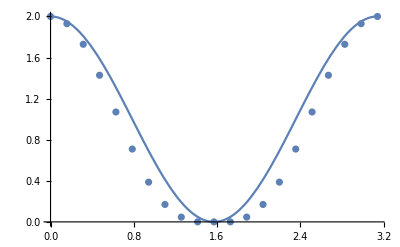

```mathematica
Show[ListPlot[tmmax],Plot[1+Cos[2x],{x,0,Pi}]]
```

```mathematica
FindFit[tmmax,y=a+b x+c x^2 + d  x^3,{a,b,c,d},x]
```

FindFit::fitd: First argument {{0,1.99999999999999978},{0.15708,1.92968032403755618},{0.314159,1.7290302048728452},{0.471239,1.42759313111027453},{0.628319,1.0700096148931344},«13»,{2.67035,1.42759313111029895},{2.82743,1.72903020487285786},{2.98451,1.92968032403755929},{π,2.}} in FindFit is not a list or a rectangular array.

FindFit[{{0,1.99999999999999978},{0.15708,1.92968032403755618},{0.314159,1.7290302048728452},{0.471239,1.42759313111027453},{0.628319,1.0700096148931344},{0.785398,0.709157805330578372},{0.942478,0.387147001070131835},{1.09956,0.169750806199618687},{1.25664,0.0465871263037743386},{1.41372,0.000431958267483941599},Null,{1.5708,1.44474535322045547×10^-13},{1.72788,0.000431958267482180204},{1.88496,0.0465871263037786407},{2.04204,0.169750806199630788},{2.19911,0.387147001070151431},{2.35619,0.70915780533060202},{2.51327,1.07000961489316593},{2.67035,1.42759313111029895},{2.82743,1.72903020487285786},{2.98451,1.92968032403755929},{π,2.}},a+b x+c x^2+d x^3,{a,b,c,d},x]

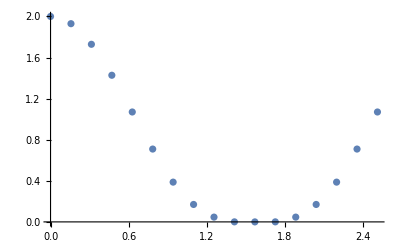

```mathematica
ListPlot[{{0,Max[tm0]},{0.05Pi,Max[tm005pi]},{0.1Pi,Max[tm01pi]},{0.15Pi,Max[tm015pi]},{0.2Pi,Max[tm02pi]},{0.25Pi,Max[tm025pi]},{0.3Pi,Max[tm03pi]},{0.35Pi,Max[tm035pi]},{0.4Pi,Max[tm04pi]},{0.45Pi,Max[tm045pi]},,{0.5Pi,Max[tm05pi]},{0.55Pi,Max[tm055pi]},{0.6Pi,Max[tm06pi]},{0.65Pi,Max[tm065pi]},{0.7Pi,Max[tm07pi]},{0.75Pi,Max[tm075pi]},{0.8Pi,Max[tm08pi]}}]
```

```mathematica
Show[%38,AxesLabel->{HoldForm[Number of kicks],HoldForm[Entanglement entropy]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gcomb: Could not combine the graphics objects in Show[{-3.20343×10^-16,0.479014,0.641017,0.840561,0.939679,1.05032,1.12739,1.21397,1.27654,1.27359,1.29808,1.31671,1.35302,1.38437,1.41429,1.41638,1.42661,1.43496,1.45053,1.50009,1.52796,1.49033,«7»,1.55312,1.57219,1.56162,1.55986,1.56978,1.58321,1.58557,1.58241,1.59202,1.59336,1.56973,1.56451,1.53573,1.54617,1.56084,1.57487,1.58926,1.59134,1.597,1.59478,1.59837,«150»},«2»,«1»].

Show[{-3.20343×10^-16,0.479014,0.641017,0.840561,0.939679,1.05032,1.12739,1.21397,1.27654,1.27359,1.29808,1.31671,1.35302,1.38437,1.41429,1.41638,1.42661,1.43496,1.45053,1.50009,1.52796,1.49033,1.4815,1.47204,1.48979,1.4954,1.50309,1.53462,1.52968,1.55312,1.57219,1.56162,1.55986,1.56978,1.58321,1.58557,1.58241,1.59202,1.59336,1.56973,1.56451,1.53573,1.54617,1.56084,1.57487,1.58926,1.59134,1.597,1.59478,1.59837,1.58694,1.60219,1.62767,1.65011,1.64186,1.61472,1.63219,1.63859,1.63727,1.63918,1.63929,1.61945,1.60476,1.60045,1.58472,1.58982,1.59057,1.62981,1.64568,1.59652,1.59559,1.62884,1.64191,1.6337,1.63512,1.67562,1.68547,1.6858,1.68953,1.66779,1.6655,1.63648,1.6294,1.64896,1.67592,1.69341,1.68762,1.71038,1.72581,1.71307,1.72941,1.72782,1.72499,1.73583,1.72897,1.70036,1.67961,1.6798,1.66888,1.65181,1.64412,1.64483,1.65036,1.65308,1.65788,1.65442,1.65112,1.64235,1.65535,1.67147,1.6644,1.65871,1.66954,1.66529,1.65635,1.67327,1.67203,1.65488,1.65173,1.65272,1.64813,1.67758,1.69986,1.68864,1.67303,1.69081,1.70059,1.68974,1.69875,1.72161,1.71846,1.68464,1.68795,1.68857,1.6958,1.69746,1.69025,1.68557,1.68314,1.69658,1.70147,1.69132,1.68045,1.65559,1.64427,1.65427,1.66563,1.69775,1.69674,1.66214,1.65892,1.64351,1.63791,1.6441,1.65411,1.65718,1.65012,1.65437,1.64677,1.65932,1.67587,1.69771,1.69159,1.6646,1.66684,1.65227,1.64898,1.66886,1.6898,1.71079,1.7136,1.71367,1.72137,1.71641,1.72581,1.72475,1.72624,1.71825,1.70446,1.69693,1.69887,1.67503,1.65978,1.63168,1.64698,1.69011,1.69449,1.68143,1.66712,1.66537,1.65556,1.64446,1.66341,1.68934,1.69043,1.68656,1.67216,1.68322,1.68099,1.67096},AxesLabel→{Number of kicks,Entanglement entropy},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

#### plotting

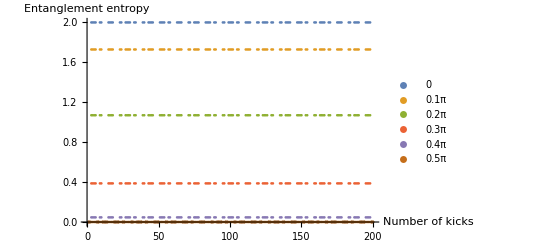

```mathematica
Show[ListPlot[{Legended[tm0,"0"],Legended[tm01pi,"0.1π"],Legended[tm02pi,"0.2π"],Legended[tm03pi,"0.3π"],Legended[tm04pi,"0.4π"],Legended[tm05pi,"0.5π"]}],AxesLabel->{HoldForm[Number of kicks],HoldForm[Entanglement entropy]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

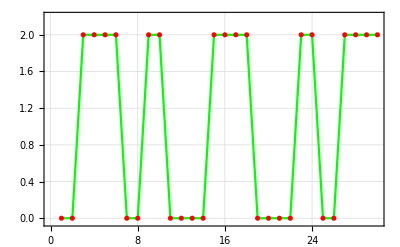

```mathematica
Show[ListLinePlot[Drop[tm0,-170],PlotStyle->Green,PlotTheme->"Detailed",PlotRange->{-0.04,2.2}],ListPlot[tm0,PlotStyle->{Thick,Red}]]
```

```mathematica
Show[%27,FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},PlotLabel->HoldForm[Thue-Morse sequence],LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]}]
```

Show::gcomb: Could not combine the graphics objects in Show[«1»].

Show[{0.,0.363089,0.415818,0.54839,0.589039,0.674437,0.70374,0.748022,0.770234,0.779996,0.79391,0.801613,0.815223,0.870347,0.884279,0.888776,0.908845,0.947454,0.957304,0.940394,0.950592,0.939182,0.94311,0.96134,0.960706,0.976041,0.987726,0.991919,0.998017,0.99818,0.998194,1.00909,1.01133,0.981512,0.987854,1.00632,1.00986,1.01646,1.01745,1.02404,1.02835,1.03458,1.04478,1.05088,1.04256,1.00897,1.00533,1.01531,1.01092,1.02858,1.02725,1.01485,1.01685,0.994844,0.989307,0.980029,0.977777,1.00867,1.00945,1.01261,1.01547,1.00462,1.01431,1.01535,1.02326,1.04083,1.03859,1.01655,1.02333,1.03903,1.04625,1.02619,1.01702,1.04774,1.04826,1.04382,1.04221,1.04813,1.04857,1.03537,1.02608,1.02969,1.03201,1.02472,1.02739,1.02287,1.02153,1.045,1.05381,1.03579,1.03515,1.02636,1.02,1.03245,1.03474,1.03434,1.02872,1.01985,1.02619,1.02418,1.02443,1.03411,1.02681,1.02347,1.02948,1.02779,1.03174,1.02573,1.02419,1.02418,1.01988,1.03808,1.05531,1.05959,1.06073,1.05268,1.05002,1.06247,1.05794,1.04193,1.05439,1.07112,1.06521,1.06354,1.06746,1.06946,1.0642,1.04648,1.0573,1.09333,1.08943,1.08936,1.10344,1.1051,1.09868,1.09257,1.09739,1.09256,1.09542,1.09635,1.08879,1.09036,1.09215,1.08421,1.07948,1.07018,1.06967,1.05433,1.05514,1.0712,1.07087,1.06858,1.0588,1.06046,1.06445,1.06252,1.06614,1.08653,1.0879,1.08935,1.09177,1.08538,1.08726,1.09208,1.08736,1.05835,1.0577,1.06509,1.05688,1.04489,1.03387,1.01525,1.02681,1.04444,1.04145,1.04933,1.04891,1.05342,1.05031,1.03502,1.03113,1.02929,1.02601,1.03449,1.04284,1.06111,1.06183,1.05389,1.05595,1.04104,1.03895,1.05551,1.0516,1.0413,1.04527,1.05286,1.06192,1.03337,1.02272,1.02559},FrameLabel→{{Entanglement entropy,None},{Number of kicks,None}},PlotLabel→Thue-Morse sequence,LabelStyle→{FontFamily→TeX Gyre Pagella,GrayLevel[0]}]

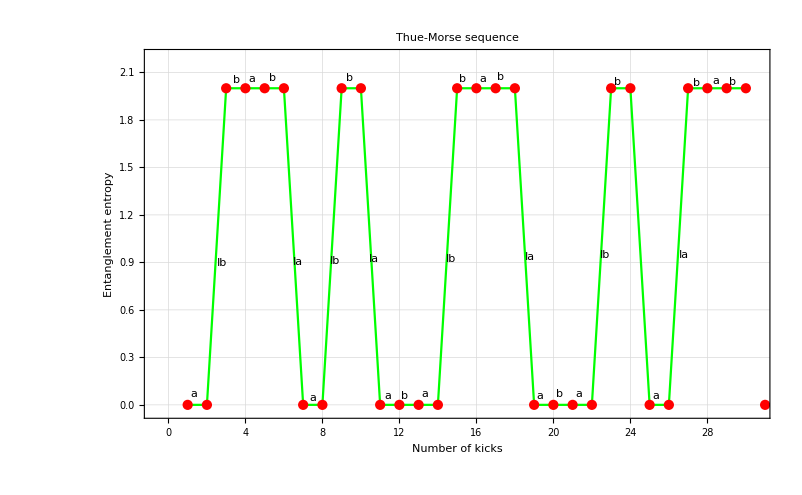

-Graphics-

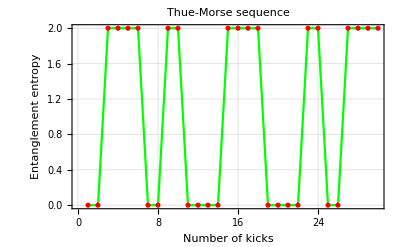

-Graphics-

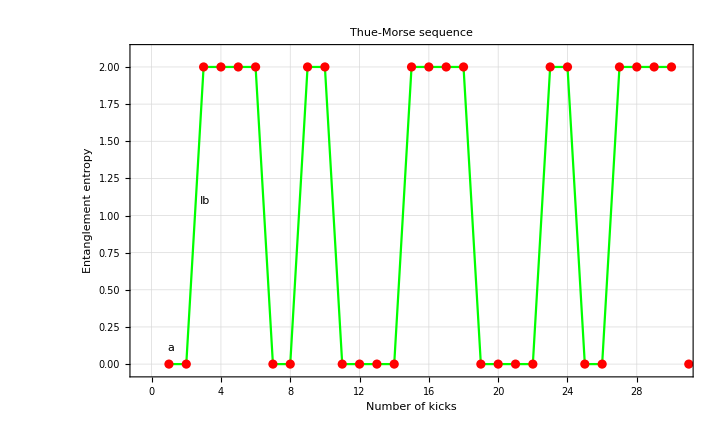

-Graphics-

```mathematica
tmmean={{0,Mean[tm0]},{0.05Pi,Mean[tm005pi]},{0.1Pi,Mean[tm01pi]},{0.15Pi,Mean[tm015pi]},{0.2Pi,Mean[tm02pi]},{0.25Pi,Mean[tm025pi]},{0.3Pi,Mean[tm03pi]},{0.35Pi,Mean[tm035pi]},{0.4Pi,Mean[tm04pi]},{0.45Pi,Mean[tm045pi]},,{0.5Pi,Mean[tm05pi]},{0.55Pi,Mean[tm055pi]},{0.6Pi,Mean[tm06pi]},{0.65Pi,Mean[tm065pi]},{0.7Pi,Mean[tm07pi]},{0.75Pi,Mean[tm075pi]},{0.8Pi,Mean[tm08pi]},{0.85Pi,Mean[tm085pi]},{0.9Pi,Mean[tm09pi]},{0.95Pi,Mean[tm095pi]},{Pi,Mean[tmpi]}}
```

{{0,1.00000000000001063},{0.15708,0.964840162018807676},{0.314159,0.864515102436438189},{0.471239,0.713796565555156708},{0.628319,0.535004807446583857},{0.785398,0.3545789026652992},{0.942478,0.193573500535071863},{1.09956,0.0848754030998117781},{1.25664,0.0232935631518883197},{1.41372,0.000215979133743255359},Null,{1.5708,7.219562×10^-14},{1.72788,0.000215979133742160671},{1.88496,0.0232935631518899932},{2.04204,0.0848754030998152963},{2.19911,0.193573500535076646},{2.35619,0.354578902665301366},{2.51327,0.535004807446583018},{2.67035,0.713796565555147692},{2.82743,0.864515102436426438},{2.98451,0.964840162018792946},{π,0.999999999999999926}}

#### Alternate spins 4 - ent entropy

```mathematica
alttm={-0.000000000000000000*10^+00,6.406853007629834296*10^-16,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.922055902288949598*10^-15,2.562741203051931746*10^-15,1.999999999999999112*10^+00,1.999999999999999112*10^+00,2.562741203051931746*10^-15,3.203426503814914288*10^-15,3.203426503814914288*10^-15,3.844111804577896041*10^-15,1.999999999999998668*10^+00,1.999999999999998224*10^+00,1.999999999999998446*10^+00,1.999999999999998446*10^+00,3.844111804577896041*10^-15,4.484797105340877400*10^-15,4.484797105340877400*10^-15,5.125482406103859548*10^-15,1.999999999999998224*10^+00,1.999999999999998002*10^+00,5.125482406103859548*10^-15,5.766167706866840118*10^-15,1.999999999999997780*10^+00,1.999999999999997780*10^+00,1.999999999999997558*10^+00,1.999999999999997780*10^+00,6.406853007629821477*10^-15,7.047538308392801258*10^-15,1.999999999999997335*10^+00,1.999999999999997335*10^+00,7.367880958774292331*10^-15,8.008566259537272901*10^-15,8.008566259537272901*10^-15,8.649251560300251894*10^-15,1.999999999999996891*10^+00,1.999999999999996447*10^+00,1.089165011297067916*10^-14,1.153233541373365815*10^-14,1.999999999999995559*10^+00,1.999999999999995337*10^+00,1.999999999999995337*10^+00,1.999999999999995337*10^+00,1.601713251907450163*10^-14,1.665781781983747589*10^-14,1.665781781983747589*10^-14,1.729850312060045014*10^-14,1.999999999999993339*10^+00,1.999999999999993339*10^+00,1.999999999999993117*10^+00,1.999999999999993339*10^+00,2.018158697403384220*10^-14,2.082227227479681646*10^-14,1.999999999999991784*10^+00,1.999999999999991784*10^+00,2.146295757555979072*10^-14,2.210364287632276498*10^-14,2.210364287632276498*10^-14,2.274432817708573608*10^-14,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999990896*10^+00,2.306467082746722163*10^-14,2.370535612823019905*10^-14,2.370535612823019905*10^-14,2.434604142899317015*10^-14,1.999999999999990674*10^+00,1.999999999999990674*10^+00,2.402569877861168144*10^-14,2.466638407937465570*10^-14,1.999999999999990674*10^+00,1.999999999999990230*10^+00,1.999999999999990674*10^+00,1.999999999999990230*10^+00,2.498672672975614125*10^-14,2.562741203051911551*10^-14,2.562741203051911551*10^-14,2.626809733128208346*10^-14,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999989564*10^+00,2.690878263204505772*10^-14,2.754946793280802882*10^-14,1.999999999999989342*10^+00,1.999999999999989342*10^+00,2.754946793280802882*10^-14,2.819015323357099993*10^-14,2.819015323357099993*10^-14,2.883083853433397103*10^-14,1.999999999999988898*10^+00,1.999999999999988898*10^+00,3.075289443662288434*10^-14,3.139357973738585544*10^-14,1.999999999999987788*10^+00,1.999999999999987788*10^+00,1.999999999999987788*10^+00,1.999999999999987566*10^+00,3.555803419234514869*10^-14,3.619871949310811348*10^-14,1.999999999999986233*10^+00,1.999999999999986233*10^+00,3.972248864730443562*10^-14,4.036317394806740041*10^-14,4.036317394806740041*10^-14,4.100385924883035889*10^-14,1.999999999999984013*10^+00,1.999999999999984457*10^+00,1.999999999999984235*10^+00,1.999999999999984235*10^+00,4.196488719997481554*10^-14,4.260557250073778034*10^-14,4.260557250073778034*10^-14,4.324625780150074513*10^-14,1.999999999999983569*10^+00,1.999999999999983569*10^+00,4.324625780150074513*10^-14,4.388694310226370361*10^-14,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999983125*10^+00,4.420728575264518285*10^-14,4.484797105340814765*10^-14,1.999999999999982681*10^+00,1.999999999999982681*10^+00,4.452762840302666840*10^-14,4.516831370378963320*10^-14,4.516831370378963320*10^-14,4.580899900455259799*10^-14,1.999999999999982236*10^+00,1.999999999999982236*10^+00,4.548865635417111875*10^-14,4.612934165493407723*10^-14,1.999999999999982236*10^+00,1.999999999999982014*10^+00,1.999999999999982014*10^+00,1.999999999999981792*10^+00,4.709036960607852126*10^-14,4.773105490684148606*10^-14,4.773105490684148606*10^-14,4.837174020760444454*10^-14,1.999999999999981348*10^+00,1.999999999999981348*10^+00,1.999999999999981126*10^+00,1.999999999999981126*10^+00,4.997345345951185337*10^-14,5.061413876027481185*10^-14,1.999999999999980238*10^+00,1.999999999999980460*10^+00,5.381756526408961688*10^-14,5.445825056485256905*10^-14,5.445825056485256905*10^-14,5.509893586561553384*10^-14,1.999999999999978684*10^+00,1.999999999999978684*10^+00,5.862270501981179918*10^-14,5.926339032057475766*10^-14,1.999999999999977129*10^+00,1.999999999999977129*10^+00,1.999999999999976907*10^+00,1.999999999999976907*10^+00,6.150578887324509973*10^-14,6.214647417400807083*10^-14,1.999999999999976019*10^+00,1.999999999999976019*10^+00,6.246681682438955007*10^-14,6.310750212515249593*10^-14,6.310750212515249593*10^-14,6.374818742591545441*10^-14,1.999999999999975575*10^+00,1.999999999999975353*10^+00,1.999999999999975131*10^+00,1.999999999999975131*10^+00,6.406853007629693365*10^-14,6.470921537705987952*10^-14,6.470921537705987952*10^-14,6.534990067782283800*10^-14,1.999999999999974909*10^+00,1.999999999999974909*10^+00,6.502955802744137138*10^-14,6.567024332820431724*10^-14,1.999999999999974687*10^+00,1.999999999999974687*10^+00,1.999999999999974465*10^+00,1.999999999999974243*10^+00,6.599058597858579648*10^-14,6.663127127934874234*10^-14,6.663127127934874234*10^-14,6.727195658011170082*10^-14,1.999999999999974021*10^+00,1.999999999999974021*10^+00,1.999999999999973799*10^+00,1.999999999999974021*10^+00,6.791264188087465930*10^-14,6.855332718163760516*10^-14,2.722912528242654327*10^-14,2.786981058318951437*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.011220913585990693*10^-14,3.075289443662288434*10^-14,1.929680324037555295*10^+00,1.929680324037555295*10^+00,3.235460768853030579*10^-14,3.299529298929327058*10^-14,3.299529298929327058*10^-14,3.363597829005624800*10^-14,1.929680324037553962*10^+00,1.929680324037553962*10^+00,1.929680324037553962*10^+00,1.929680324037553962*10^+00,3.635889081829885941*10^-14,3.699957611906182420*10^-14,3.699957611906182420*10^-14,3.764026141982478899*10^-14,1.929680324037552630*10^+00,1.929680324037552630*10^+00,4.036317394806740041*10^-14,4.100385924883035889*10^-14,1.929680324037551298*10^+00,1.929680324037551298*10^+00,1.929680324037551298*10^+00,1.929680324037551298*10^+00,4.308608647630999920*10^-14,4.372677177707296399*10^-14,1.929680324037550410*10^+00,1.929680324037550188*10^+00,4.516831370378963320*10^-14,4.612934165493407723*10^-14,4.612934165493407723*10^-14,4.677002695569704202*10^-14,1.929680324037549077*10^+00,1.929680324037549077*10^+00,4.805139755722296530*10^-14,4.869208285798593009*10^-14,1.929680324037548633*10^+00,1.929680324037548633*10^+00,1.929680324037548633*10^+00,1.929680324037548633*10^+00,5.029379610989333261*10^-14,5.093448141065629109*10^-14,5.093448141065629109*10^-14,5.141499538622851626*10^-14,1.929680324037547523*10^+00,1.929680324037547745*10^+00,1.929680324037547523*10^+00,1.929680324037547523*10^+00,5.365739393889887726*10^-14,5.445825056485256905*10^-14,1.929680324037546857*10^+00,1.929680324037546413*10^+00,5.589979249156923194*10^-14,5.654047779233219043*10^-14,5.654047779233219043*10^-14,5.718116309309514260*10^-14,1.929680324037545747*10^+00,1.929680324037545747*10^+00,1.929680324037545525*10^+00,1.929680324037545747*10^+00,5.894304767019327842*10^-14,5.958373297095623690*10^-14,5.958373297095623690*10^-14,6.022441827171919539*10^-14,1.929680324037544414*10^+00,1.929680324037544636*10^+00,6.246681682438955007*10^-14,6.310750212515249593*10^-14,1.929680324037543526*10^+00,1.929680324037543526*10^+00,1.929680324037543304*10^+00,1.929680324037543526*10^+00,6.567024332820431724*10^-14,6.631092862896727572*10^-14,6.631092862896727572*10^-14,6.695161392973023420*10^-14,1.929680324037541972*10^+00,1.929680324037541972*10^+00,1.929680324037541972*10^+00,1.929680324037541972*10^+00,6.935418380759130326*10^-14,6.999486910835424912*10^-14,1.929680324037540862*10^+00,1.929680324037540862*10^+00,7.191692501064311195*10^-14,7.255761031140605781*10^-14,7.255761031140605781*10^-14,7.319829561216901629*10^-14,1.929680324037539751*10^+00,1.929680324037539751*10^+00,7.544069416483933311*10^-14,7.608137946560229159*10^-14,1.929680324037538863*10^+00,1.929680324037538863*10^+00,1.929680324037538419*10^+00,1.929680324037538863*10^+00,7.816360669308186879*10^-14,7.880429199384482728*10^-14,1.929680324037537753*10^+00,1.929680324037537753*10^+00,8.040600524575219824*10^-14,8.104669054651513147*10^-14,8.104669054651513147*10^-14,8.152720452208735034*10^-14,1.929680324037536643*10^+00,1.929680324037537087*10^+00,1.929680324037536643*10^+00,1.929680324037536643*10^+00,8.392977439994839416*10^-14,8.457045970071134002*10^-14,8.457045970071134002*10^-14,8.521114500147428588*10^-14,1.929680324037535311*10^+00,1.929680324037535311*10^+00,8.617217295261871098*10^-14,8.681285825338165684*10^-14,1.929680324037534866*10^+00,1.929680324037534422*10^+00,1.929680324037534866*10^+00,1.929680324037534422*10^+00,8.921542813124270066*10^-14,8.985611343200564652*10^-14,1.929680324037533534*10^+00,1.929680324037533534*10^+00,9.113748403353152562*10^-14,9.193834065948521110*10^-14,9.193834065948521110*10^-14,9.257902596024814433*10^-14,1.929680324037533090*10^+00,1.929680324037532646*10^+00,9.466125318772770891*10^-14,9.514176716329991515*10^-14,1.929680324037531314*10^+00,1.929680324037531758*10^+00,1.929680324037531314*10^+00,1.929680324037531314*10^+00,9.738416571597020673*10^-14,9.802485101673315259*10^-14,9.802485101673315259*10^-14,9.866553631749608583*10^-14,1.929680324037530426*10^+00,1.929680324037530426*10^+00,1.929680324037529981*10^+00,1.929680324037530426*10^+00,1.005875922197848982*10^-13,1.012282775205478440*10^-13,1.929680324037529537*10^+00,1.929680324037529981*10^+00,1.028299907724551897*10^-13,1.034706760732181356*10^-13,1.034706760732181356*10^-13,1.039511900487903418*10^-13,1.929680324037528427*10^+00,1.929680324037528649*10^+00,1.060334172762698812*10^-13,1.066741025770328144*10^-13,1.929680324037527317*10^+00,1.929680324037527761*10^+00,1.929680324037527317*10^+00,1.929680324037527317*10^+00,1.089165011297030934*10^-13,1.095571864304660266*10^-13,1.929680324037526429*10^+00,1.929680324037526429*10^+00,1.114792423327548389*10^-13,1.121199276335177722*10^-13,1.121199276335177722*10^-13,1.127606129342807054*10^-13,1.929680324037525541*10^+00,1.929680324037525097*10^+00,1.929680324037525541*10^+00,1.929680324037525097*10^+00,1.156436967877139050*10^-13,1.164445534136675652*10^-13,1.164445534136675652*10^-13,1.169250673892397715*10^-13,1.929680324037523764*10^+00,1.929680324037523764*10^+00,1.185267806411470667*10^-13,1.191674659419100252*10^-13,1.929680324037522876*10^+00,1.929680324037523098*10^+00,1.929680324037522432*10^+00,1.929680324037522876*10^+00,1.207691791938173457*10^-13,1.215700358197710059*10^-13,1.215700358197710059*10^-13,1.222107211205339391*10^-13,1.929680324037521988*10^+00,1.929680324037521988*10^+00,1.929680324037521766*10^+00,1.929680324037521766*10^+00,1.247734623235856721*10^-13,1.254141476243485801*10^-13,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,1.729030204872844978*10^+00,1.729030204872844978*10^+00,1.729030204872844978*10^+00,1.729030204872845200*10^+00,3.203426503814917641*10^-16,1.281370601525966465*10^-15,1.729030204872844756*10^+00,1.729030204872845200*10^+00,2.082227227479694741*10^-15,2.883083853433422820*10^-15,2.722912528242677283*10^-15,3.523769154196404968*10^-15,1.729030204872844312*10^+00,1.729030204872844312*10^+00,1.729030204872844312*10^+00,1.729030204872844312*10^+00,4.324625780150133047*10^-15,4.965311080913113616*10^-15,4.965311080913113616*10^-15,5.766167706866840118*10^-15,1.729030204872843646*10^+00,1.729030204872843646*10^+00,5.926339032057585260*10^-15,6.567024332820566619*10^-15,1.729030204872843868*10^+00,1.729030204872843424*10^+00,1.729030204872843424*10^+00,1.729030204872843424*10^+00,7.848394934346526970*10^-15,8.489080235109505962*10^-15,1.729030204872843202*10^+00,1.729030204872842980*10^+00,1.041113613739844452*10^-14,1.121199276335216944*10^-14,1.121199276335216944*10^-14,1.185267806411514685*10^-14,1.729030204872842091*10^+00,1.729030204872841869*10^+00,1.393490529159482503*10^-14,1.441541926716705493*10^-14,1.729030204872841425*10^+00,1.729030204872840981*10^+00,1.729030204872841647*10^+00,1.729030204872841647*10^+00,1.729850312060045014*10^-14,1.793918842136342756*10^-14,1.793918842136342756*10^-14,1.874004504731714775*10^-14,1.729030204872840315*10^+00,1.729030204872840315*10^+00,1.729030204872839871*10^+00,1.729030204872839871*10^+00,2.098244359998755608*10^-14,2.146295757555979072*10^-14,1.729030204872839205*10^+00,1.729030204872839205*10^+00,2.386552745342093867*10^-14,2.450621275418391293*10^-14,2.466638407937465570*10^-14,2.530706938013762680*10^-14,1.729030204872837873*10^+00,1.729030204872838095*10^+00,1.729030204872837650*10^+00,1.729030204872838095*10^+00,2.674861130685431494*10^-14,2.738929660761728605*10^-14,2.738929660761728605*10^-14,2.786981058318951437*10^-14,1.729030204872837206*10^+00,1.729030204872837206*10^+00,2.899100985952471696*10^-14,2.963169516028768807*10^-14,1.729030204872836762*10^+00,1.729030204872837206*10^+00,1.729030204872836540*10^+00,1.729030204872836762*10^+00,3.219443636333955986*10^-14,3.283512166410253727*10^-14,3.299529298929327058*10^-14,3.347580696486550206*10^-14,1.729030204872835874*10^+00,1.729030204872835874*10^+00,1.729030204872835874*10^+00,1.729030204872835652*10^+00,3.651906214348960534*10^-14,3.715974744425256382*10^-14,1.729030204872834764*10^+00,1.729030204872834986*10^+00,3.892163202135072489*10^-14,3.972248864730443562*10^-14,3.972248864730443562*10^-14,4.020300262287665448*10^-14,1.729030204872833654*10^+00,1.729030204872834098*10^+00,4.196488719997481554*10^-14,4.260557250073778034*10^-14,1.729030204872832988*10^+00,1.729030204872832988*10^+00,1.729030204872832543*10^+00,1.729030204872833210*10^+00,4.452762840302666840*10^-14,4.500814237859889358*10^-14,1.729030204872832321*10^+00,1.729030204872832099*10^+00,4.677002695569704202*10^-14,4.741071225646000051*10^-14,4.741071225646000051*10^-14,4.805139755722296530*10^-14,1.729030204872831433*10^+00,1.729030204872831433*10^+00,1.729030204872831433*10^+00,1.729030204872831433*10^+00,5.013362478470259299*10^-14,5.093448141065629109*10^-14,5.077431008546555147*10^-14,5.141499538622851626*10^-14,1.729030204872830323*10^+00,1.729030204872830323*10^+00,5.301670863813591247*10^-14,5.349722261370813764*10^-14,1.729030204872829657*10^+00,1.729030204872829657*10^+00,1.729030204872829657*10^+00,1.729030204872829435*10^+00,5.638030646714145081*10^-14,5.702099176790440298*10^-14,1.729030204872828769*10^+00,1.729030204872828547*10^+00,5.910321899538401804*10^-14,5.974390429614697652*10^-14,5.974390429614697652*10^-14,6.038458959690993501*10^-14,1.729030204872827658*10^+00,1.729030204872827436*10^+00,6.278715947477102931*10^-14,6.326767345034323555*10^-14,1.729030204872826770*10^+00,1.729030204872826770*10^+00,1.729030204872826326*10^+00,1.729030204872826770*10^+00,6.502955802744137138*10^-14,6.551007200301357762*10^-14,6.551007200301357762*10^-14,6.615075730377653610*10^-14,1.729030204872825660*10^+00,1.729030204872825882*10^+00,1.729030204872825882*10^+00,1.729030204872825438*10^+00,6.743212790530244044*10^-14,6.855332718163760516*10^-14,1.729030204872825216*10^+00,1.729030204872825216*10^+00,7.015504043354500137*10^-14,7.063555440911720761*10^-14,7.063555440911720761*10^-14,7.143641103507089309*10^-14,1.729030204872824328*10^+00,1.729030204872824106*10^+00,7.335846693735974329*10^-14,7.383898091293196215*10^-14,1.729030204872823440*10^+00,1.729030204872823440*10^+00,1.729030204872823440*10^+00,1.729030204872823440*10^+00,7.576103681522081235*10^-14,7.656189344117449783*10^-14,1.729030204872822996*10^+00,1.729030204872822996*10^+00,7.784326404270040217*10^-14,7.864412066865407503*10^-14,7.864412066865407503*10^-14,7.912463464422629389*10^-14,1.729030204872821663*10^+00,1.729030204872821885*10^+00,1.729030204872821663*10^+00,1.729030204872821885*10^+00,8.152720452208735034*10^-14,8.232806114804103582*10^-14,8.232806114804103582*10^-14,8.296874644880398168*10^-14,1.729030204872820775*10^+00,1.729030204872821219*10^+00,8.473063102590209226*10^-14,8.537131632666503812*10^-14,1.729030204872820331*10^+00,1.729030204872820331*10^+00,1.729030204872820331*10^+00,1.729030204872820331*10^+00,8.617217295261871098*10^-14,8.681285825338165684*10^-14,8.681285825338165684*10^-14,8.729337222895387570*10^-14,1.729030204872819665*10^+00,1.729030204872819665*10^+00,1.729030204872819665*10^+00,1.729030204872819221*10^+00,8.921542813124270066*10^-14,8.985611343200564652*10^-14,9.610279511444749964*10^-16,1.761884577098203667*10^-15,1.427593131110274083*10^+00,1.427593131110274527*10^+00,1.427593131110274083*10^+00,1.427593131110274527*10^+00,4.164454454959387115*10^-15,4.805139755722368474*10^-15,1.427593131110274083*10^+00,1.427593131110274083*10^+00,6.727195658011310973*10^-15,7.528052283965036685*10^-15,7.528052283965036685*10^-15,8.328908909918763186*10^-15,1.427593131110272751*10^+00,1.427593131110272751*10^+00,1.427593131110272973*10^+00,1.427593131110272973*10^+00,9.770450836635465524*10^-15,1.057130746258919045*10^-14,1.057130746258919045*10^-14,1.105182143816142351*10^-14,1.427593131110272751*10^+00,1.427593131110272306*10^+00,1.233319203968737992*10^-14,1.297387734045035891*10^-14,1.427593131110272529*10^+00,1.427593131110272084*10^+00,1.427593131110272306*10^+00,1.427593131110272306*10^+00,1.441541926716705493*10^-14,1.521627589312077828*10^-14,1.427593131110272751*10^+00,1.427593131110272529*10^+00,1.697816047021896459*10^-14,1.793918842136342756*10^-14,1.793918842136342756*10^-14,1.874004504731714775*10^-14,1.427593131110271418*10^+00,1.427593131110271640*10^+00,2.082227227479681646*10^-14,2.146295757555979072*10^-14,1.427593131110270974*10^+00,1.427593131110271418*10^+00,1.427593131110270974*10^+00,1.427593131110270974*10^+00,2.306467082746722163*10^-14,2.354518480303945311*10^-14,2.370535612823019905*10^-14,2.418587010380242737*10^-14,1.427593131110270752*10^+00,1.427593131110270974*10^+00,1.427593131110270752*10^+00,1.427593131110270752*10^+00,2.594775468090060106*10^-14,2.674861130685431494*10^-14,1.427593131110270530*10^+00,1.427593131110270530*10^+00,2.802998190838025715*10^-14,2.851049588395248548*10^-14,2.867066720914323141*10^-14,2.915118118471545658*10^-14,1.427593131110270308*10^+00,1.427593131110270308*10^+00,1.427593131110270308*10^+00,1.427593131110270086*10^+00,3.107323708700436989*10^-14,3.171392238776734100*10^-14,3.187409371295807431*10^-14,3.235460768853030579*10^-14,1.427593131110269642*10^+00,1.427593131110269420*10^+00,3.299529298929327058*10^-14,3.363597829005624800*10^-14,1.427593131110269642*10^+00,1.427593131110269198*10^+00,1.427593131110269642*10^+00,1.427593131110269198*10^+00,3.507752021677292351*10^-14,3.587837684272663424*10^-14,3.587837684272663424*10^-14,3.651906214348960534*10^-14,1.427593131110269198*10^+00,1.427593131110269198*10^+00,1.427593131110269198*10^+00,1.427593131110269198*10^+00,3.844111804577849972*10^-14,3.908180334654146451*10^-14,1.427593131110268976*10^+00,1.427593131110268976*10^+00,4.036317394806740041*10^-14,4.084368792363962558*10^-14,4.084368792363962558*10^-14,4.164454454959332999*10^-14,1.427593131110268310*10^+00,1.427593131110268532*10^+00,4.292591515111925958*10^-14,4.356660045188222437*10^-14,1.427593131110268088*10^+00,1.427593131110268310*10^+00,1.427593131110268088*10^+00,1.427593131110268088*10^+00,4.484797105340814765*10^-14,4.564882767936185206*10^-14,1.427593131110268310*10^+00,1.427593131110267866*10^+00,4.677002695569704202*10^-14,4.741071225646000051*10^-14,4.757088358165074013*10^-14,4.789122623203222568*10^-14,1.427593131110267866*10^+00,1.427593131110267866*10^+00,1.427593131110267866*10^+00,1.427593131110267866*10^+00,4.997345345951185337*10^-14,5.061413876027481185*10^-14,5.077431008546555147*10^-14,5.141499538622851626*10^-14,1.427593131110267421*10^+00,1.427593131110267199*10^+00,5.333705128851739802*10^-14,5.397773658928035019*10^-14,1.427593131110267421*10^+00,1.427593131110266977*10^+00,1.427593131110266977*10^+00,1.427593131110267199*10^+00,5.654047779233219043*10^-14,5.702099176790440298*10^-14,1.427593131110266533*10^+00,1.427593131110266533*10^+00,5.782184839385810108*10^-14,5.862270501981179918*10^-14,5.862270501981179918*10^-14,5.926339032057475766*10^-14,1.427593131110266311*10^+00,1.427593131110266311*10^+00,6.070493224729141425*10^-14,6.118544622286362049*10^-14,1.427593131110265867*10^+00,1.427593131110265645*10^+00,1.427593131110266089*10^+00,1.427593131110265867*10^+00,6.374818742591545441*10^-14,6.422870140148766065*10^-14,6.438887272667840027*10^-14,6.502955802744137138*10^-14,1.427593131110265423*10^+00,1.427593131110265201*10^+00,1.427593131110265645*10^+00,1.427593131110265423*10^+00,6.711178525492097382*10^-14,6.759229923049318006*10^-14,1.427593131110265201*10^+00,1.427593131110264979*10^+00,6.919401248240056364*10^-14,6.951435513278204289*10^-14,6.967452645797276988*10^-14,7.015504043354500137*10^-14,1.427593131110264757*10^+00,1.427593131110264757*10^+00,7.175675368545237233*10^-14,7.207709633583385157*10^-14,1.427593131110265201*10^+00,1.427593131110264757*10^+00,1.427593131110264757*10^+00,1.427593131110264757*10^+00,7.399915223812270177*10^-14,7.463983753888564763*10^-14,1.427593131110264313*10^+00,1.427593131110264313*10^+00,7.640172211598375821*10^-14,7.688223609155597707*10^-14,7.704240741674671669*10^-14,7.784326404270040217*10^-14,1.427593131110264313*10^+00,1.427593131110263869*10^+00,1.427593131110264091*10^+00,1.427593131110264091*10^+00,7.912463464422629389*10^-14,7.976531994498925238*10^-14,7.976531994498925238*10^-14,8.040600524575219824*10^-14,1.427593131110263647*10^+00,1.427593131110263869*10^+00,8.248823247323176282*10^-14,8.312891777399472130*10^-14,1.427593131110262981*10^+00,1.427593131110262981*10^+00,1.427593131110263425*10^+00,1.427593131110262981*10^+00,8.521114500147428588*10^-14,8.601200162742798398*10^-14,8.617217295261871098*10^-14,8.649251560300017760*10^-14,1.427593131110262537*10^+00,1.427593131110262759*10^+00,1.427593131110262537*10^+00,1.427593131110262537*10^+00,8.809422885490754856*10^-14,8.873491415567049442*10^-14,4.805139755722374982*10^-16,1.281370601525966465*10^-15,1.070009614893122629*10^+00,1.070009614893122407*10^+00,1.070009614893122407*10^+00,1.070009614893122407*10^+00,3.203426503814914288*10^-15,3.844111804577896041*10^-15,1.070009614893122851*10^+00,1.070009614893122851*10^+00,5.605996381676094975*10^-15,6.086510357248330403*10^-15,5.926339032057585260*10^-15,6.567024332820566619*10^-15,1.070009614893123295*10^+00,1.070009614893122629*10^+00,1.070009614893122851*10^+00,1.070009614893122851*10^+00,8.168737584728017255*10^-15,8.969594210681742179*10^-15,8.809422885490996247*10^-15,9.289936861063230886*10^-15,1.070009614893122851*10^+00,1.070009614893123295*10^+00,1.041113613739844452*10^-14,1.121199276335216944*10^-14,1.070009614893123295*10^+00,1.070009614893123295*10^+00,1.070009614893123295*10^+00,1.070009614893123295*10^+00,1.217302071449663556*10^-14,1.281370601525961455*10^-14,1.070009614893123739*10^+00,1.070009614893123961*10^+00,1.393490529159482503*10^-14,1.473576191754854364*10^-14,1.457559059235780087*10^-14,1.521627589312077828*10^-14,1.070009614893124184*10^+00,1.070009614893124628*10^+00,1.665781781983747589*10^-14,1.729850312060045014*10^-14,1.070009614893124850*10^+00,1.070009614893124628*10^+00,1.070009614893124850*10^+00,1.070009614893124628*10^+00,1.922055902288937923*10^-14,1.954090167327086478*10^-14,1.954090167327086478*10^-14,2.002141564884309627*10^-14,1.070009614893125294*10^+00,1.070009614893125294*10^+00,1.070009614893125072*10^+00,1.070009614893124850*10^+00,2.146295757555979072*10^-14,2.178330022594127627*10^-14,1.070009614893125072*10^+00,1.070009614893125072*10^+00,2.274432817708573608*10^-14,2.338501347784871034*10^-14,2.338501347784871034*10^-14,2.354518480303945311*10^-14,1.070009614893126182*10^+00,1.070009614893125960*10^+00,1.070009614893125960*10^+00,1.070009614893126626*10^+00,2.610792600609134068*10^-14,2.674861130685431494*10^-14,2.658843998166357217*10^-14,2.690878263204505772*10^-14,1.070009614893126182*10^+00,1.070009614893126848*10^+00,2.786981058318951437*10^-14,2.835032455876174270*10^-14,1.070009614893127292*10^+00,1.070009614893127292*10^+00,1.070009614893127070*10^+00,1.070009614893127292*10^+00,3.011220913585990693*10^-14,3.059272311143213841*10^-14,3.043255178624139248*10^-14,3.107323708700436989*10^-14,1.070009614893127292*10^+00,1.070009614893127736*10^+00,1.070009614893127514*10^+00,1.070009614893127292*10^+00,3.299529298929327058*10^-14,3.363597829005624800*10^-14,1.070009614893127736*10^+00,1.070009614893127736*10^+00,3.491734889158217758*10^-14,3.555803419234514869*10^-14,3.539786286715440275*10^-14,3.619871949310811348*10^-14,1.070009614893127958*10^+00,1.070009614893128402*10^+00,3.780043274501553493*10^-14,3.812077539539701417*10^-14,1.070009614893128402*10^+00,1.070009614893127958*10^+00,1.070009614893127958*10^+00,1.070009614893128624*10^+00,4.036317394806740041*10^-14,4.068351659844887965*10^-14,1.070009614893129291*10^+00,1.070009614893129068*10^+00,4.196488719997481554*10^-14,4.244540117554703441*10^-14,4.244540117554703441*10^-14,4.324625780150074513*10^-14,1.070009614893129068*10^+00,1.070009614893129513*10^+00,1.070009614893129513*10^+00,1.070009614893129068*10^+00,4.516831370378963320*10^-14,4.580899900455259799*10^-14,4.580899900455259799*10^-14,4.612934165493407723*10^-14,1.070009614893129957*10^+00,1.070009614893129068*10^+00,4.821156888241370492*10^-14,4.869208285798593009*10^-14,1.070009614893129957*10^+00,1.070009614893129513*10^+00,1.070009614893130179*10^+00,1.070009614893130179*10^+00,5.029379610989333261*10^-14,5.061413876027481185*10^-14,1.070009614893129957*10^+00,1.070009614893130401*10^+00,5.173533803660999550*10^-14,5.253619466256369360*10^-14,5.237602333737295398*10^-14,5.301670863813591247*10^-14,1.070009614893130401*10^+00,1.070009614893130179*10^+00,5.445825056485256905*10^-14,5.509893586561553384*10^-14,1.070009614893130401*10^+00,1.070009614893130401*10^+00,1.070009614893130845*10^+00,1.070009614893130401*10^+00,5.670064911752293005*10^-14,5.734133441828588222*10^-14,5.718116309309514260*10^-14,5.782184839385810108*10^-14,1.070009614893130623*10^+00,1.070009614893131067*10^+00,1.070009614893130623*10^+00,1.070009614893130623*10^+00,5.942356164576549728*10^-14,6.006424694652845577*10^-14,1.070009614893131289*10^+00,1.070009614893131289*10^+00,6.150578887324509973*10^-14,6.214647417400807083*10^-14,6.182613152362659159*10^-14,6.262698814958028969*10^-14,1.070009614893131733*10^+00,1.070009614893131955*10^+00,6.342784477553397517*10^-14,6.422870140148766065*10^-14,1.070009614893131733*10^+00,1.070009614893131955*10^+00,1.070009614893131955*10^+00,1.070009614893131955*10^+00,6.534990067782283800*10^-14,6.599058597858579648*10^-14,1.070009614893132177*10^+00,1.070009614893132621*10^+00,6.695161392973023420*10^-14,6.743212790530244044*10^-14,6.743212790530244044*10^-14,6.791264188087465930*10^-14,1.070009614893133287*10^+00,1.070009614893132843*10^+00,1.070009614893133509*10^+00,1.070009614893133065*10^+00,6.983469778316350950*10^-14,7.015504043354500137*10^-14,7.031521175873572837*10^-14,7.063555440911720761*10^-14,1.070009614893133731*10^+00,1.070009614893133287*10^+00,7.223726766102457857*10^-14,7.271778163659681005*10^-14,1.070009614893133731*10^+00,1.070009614893133287*10^+00,1.070009614893133509*10^+00,1.070009614893133287*10^+00,7.447966621369490801*10^-14,7.480000886407638725*10^-14,7.512035151445786649*10^-14,7.560086549003007273*10^-14,1.070009614893134176*10^+00,1.070009614893134398*10^+00,1.070009614893133953*10^+00,1.070009614893134176*10^+00,7.704240741674671669*10^-14,7.752292139231892293*10^-14,3.203426503814917641*10^-16,3.203426503814917641*10^-16,7.091578053305395146*10^-01,7.091578053305402918*10^-01,7.091578053305399587*10^-01,7.091578053305405138*10^-01,2.562741203051931746*10^-15,3.203426503814914288*10^-15,7.091578053305408469*10^-01,7.091578053305411800*10^-01,4.324625780150133047*10^-15,5.125482406103859548*10^-15,4.805139755722368474*10^-15,5.605996381676094975*10^-15,7.091578053305428453*10^-01,7.091578053305427343*10^-01,7.091578053305434004*10^-01,7.091578053305430673*10^-01,7.207709633583546400*10^-15,8.008566259537272901*10^-15,7.848394934346526970*10^-15,8.649251560300251894*10^-15,7.091578053305436224*10^-01,7.091578053305442886*10^-01,9.450108186253976817*10^-15,9.770450836635465524*10^-15,7.091578053305450657*10^-01,7.091578053305449547*10^-01,7.091578053305457319*10^-01,7.091578053305451768*10^-01,1.153233541373365815*10^-14,1.233319203968737992*10^-14,7.091578053305462870*10^-01,7.091578053305462870*10^-01,1.377473396640408068*10^-14,1.457559059235780087*10^-14,1.441541926716705493*10^-14,1.489593324273928957*10^-14,7.091578053305472862*10^-01,7.091578053305471752*10^-01,1.649764649464672995*10^-14,1.697816047021896459*10^-14,7.091578053305487295*10^-01,7.091578053305480633*10^-01,7.091578053305485074*10^-01,7.091578053305482854*10^-01,1.825953107174491627*10^-14,1.890021637250789053*10^-14,1.890021637250789053*10^-14,1.938073034808011885*10^-14,7.091578053305491736*10^-01,7.091578053305493956*10^-01,7.091578053305493956*10^-01,7.091578053305497287*10^-01,2.050192962441532775*10^-14,2.114261492517830201*10^-14,7.091578053305505058*10^-01,7.091578053305507279*10^-01,2.274432817708573608*10^-14,2.322484215265796756*10^-14,2.322484215265796756*10^-14,2.370535612823019905*10^-14,7.091578053305517271*10^-01,7.091578053305519491*10^-01,7.091578053305517271*10^-01,7.091578053305518381*10^-01,2.594775468090060106*10^-14,2.610792600609134068*10^-14,2.642826865647282939*10^-14,2.674861130685431494*10^-14,7.091578053305532814*10^-01,7.091578053305531704*10^-01,2.819015323357099993*10^-14,2.867066720914323141*10^-14,7.091578053305542806*10^-01,7.091578053305538365*10^-01,7.091578053305547247*10^-01,7.091578053305541696*10^-01,3.075289443662288434*10^-14,3.123340841219510951*10^-14,3.107323708700436989*10^-14,3.155375106257659506*10^-14,7.091578053305555018*10^-01,7.091578053305551688*10^-01,7.091578053305553908*10^-01,7.091578053305552798*10^-01,3.331563563967475613*10^-14,3.395632094043772724*10^-14,7.091578053305561680*10^-01,7.091578053305559459*10^-01,3.507752021677292351*10^-14,3.555803419234514869*10^-14,3.555803419234514869*10^-14,3.619871949310811348*10^-14,7.091578053305580553*10^-01,7.091578053305572782*10^-01,3.780043274501553493*10^-14,3.844111804577849972*10^-14,7.091578053305582774*10^-01,7.091578053305584994*10^-01,7.091578053305584994*10^-01,7.091578053305586105*10^-01,4.004283129768591486*10^-14,4.036317394806740041*10^-14,7.091578053305596097*10^-01,7.091578053305592766*10^-01,4.196488719997481554*10^-14,4.260557250073778034*10^-14,4.260557250073778034*10^-14,4.292591515111925958*10^-14,7.091578053305610529*10^-01,7.091578053305609419*10^-01,7.091578053305606089*10^-01,7.091578053305610529*10^-01,4.500814237859889358*10^-14,4.564882767936185206*10^-14,4.548865635417111875*10^-14,4.580899900455259799*10^-14,7.091578053305619411*10^-01,7.091578053305622742*10^-01,4.741071225646000051*10^-14,4.805139755722296530*10^-14,7.091578053305632734*10^-01,7.091578053305631624*10^-01,7.091578053305634954*10^-01,7.091578053305640505*10^-01,4.965311080913036781*10^-14,4.997345345951185337*10^-14,7.091578053305647167*10^-01,7.091578053305641616*10^-01,5.125482406103777033*10^-14,5.205568068699146843*10^-14,5.189550936180072881*10^-14,5.253619466256369360*10^-14,7.091578053305659379*10^-01,7.091578053305662710*10^-01,5.413790791447108981*10^-14,5.477859321523404829*10^-14,7.091578053305670482*10^-01,7.091578053305669371*10^-01,7.091578053305670482*10^-01,7.091578053305668261*10^-01,5.605996381675997156*10^-14,5.686082044271366336*10^-14,5.686082044271366336*10^-14,5.750150574347662184*10^-14,7.091578053305681584*10^-01,7.091578053305682694*10^-01,7.091578053305681584*10^-01,7.091578053305684914*10^-01,5.974390429614697652*10^-14,6.022441827171919539*10^-14,7.091578053305692686*10^-01,7.091578053305694906*10^-01,6.182613152362659159*10^-14,6.230664549919881045*10^-14,6.246681682438955007*10^-14,6.294733079996175631*10^-14,7.091578053305712670*10^-01,7.091578053305707119*10^-01,6.438887272667840027*10^-14,6.454904405186913989*10^-14,7.091578053305713780*10^-01,7.091578053305719331*10^-01,7.091578053305717111*10^-01,7.091578053305720442*10^-01,6.631092862896727572*10^-14,6.663127127934874234*10^-14,7.091578053305725993*10^-01,7.091578053305722662*10^-01,6.823298453125612592*10^-14,6.855332718163760516*10^-14,6.855332718163760516*10^-14,6.903384115720982402*10^-14,7.091578053305734874*10^-01,7.091578053305737095*10^-01,7.091578053305739315*10^-01,7.091578053305735985*10^-01,7.079572573430794723*10^-14,7.127623970988015347*10^-14,7.127623970988015347*10^-14,7.159658236026163271*10^-14,7.091578053305751528*10^-01,7.091578053305750418*10^-01,7.303812428697827667*10^-14,7.367880958774122253*10^-14,7.091578053305764850*10^-01,7.091578053305760410*10^-01,7.091578053305769291*10^-01,7.091578053305761520*10^-01,7.544069416483933311*10^-14,7.624155079079303121*10^-14,7.624155079079303121*10^-14,7.656189344117449783*10^-14,7.091578053305775953*10^-01,7.091578053305782614*10^-01,7.091578053305777063*10^-01,7.091578053305783724*10^-01,7.864412066865407503*10^-14,7.912463464422629389*10^-14,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,3.871470010700654996*10^-01,3.871470010700654441*10^-01,3.871470010700660547*10^-01,3.871470010700656661*10^-01,1.601713251907457933*10^-15,2.562741203051931746*10^-15,3.871470010700672759*10^-01,3.871470010700674980*10^-01,4.164454454959387115*10^-15,4.805139755722368474*10^-15,4.805139755722368474*10^-15,5.125482406103859548*10^-15,3.871470010700689413*10^-01,3.871470010700694964*10^-01,3.871470010700695519*10^-01,3.871470010700699405*10^-01,7.367880958774292331*10^-15,7.688223609155782616*10^-15,8.008566259537272901*10^-15,8.328908909918763186*10^-15,3.871470010700718278*10^-01,3.871470010700724385*10^-01,9.930622161826211456*10^-15,1.041113613739844452*10^-14,3.871470010700737152*10^-01,3.871470010700741593*10^-01,3.871470010700741593*10^-01,3.871470010700743813*10^-01,1.313404866564110168*10^-14,1.345439131602259039*10^-14,3.871470010700763797*10^-01,3.871470010700761022*10^-01,1.537644721831152421*10^-14,1.601713251907450163*10^-14,1.601713251907450163*10^-14,1.633747516945598718*10^-14,3.871470010700779896*10^-01,3.871470010700783781*10^-01,1.825953107174491627*10^-14,1.825953107174491627*10^-14,3.871470010700794884*10^-01,3.871470010700791553*10^-01,3.871470010700802100*10^-01,3.871470010700797104*10^-01,2.098244359998755608*10^-14,2.146295757555979072*10^-14,2.146295757555979072*10^-14,2.210364287632276498*10^-14,3.871470010700825970*10^-01,3.871470010700820419*10^-01,3.871470010700825970*10^-01,3.871470010700827080*10^-01,2.402569877861168144*10^-14,2.450621275418391293*10^-14,3.871470010700839293*10^-01,3.871470010700837627*10^-01,2.626809733128208346*10^-14,2.690878263204505772*10^-14,2.722912528242654327*10^-14,2.738929660761728605*10^-14,3.871470010700865938*10^-01,3.871470010700870934*10^-01,3.871470010700866493*10^-01,3.871470010700869824*10^-01,2.947152383509694213*10^-14,2.979186648547842769*10^-14,3.011220913585990693*10^-14,3.027238046105065286*10^-14,3.871470010700888698*10^-01,3.871470010700888142*10^-01,3.203426503814882024*10^-14,3.267495033891179134*10^-14,3.871470010700909237*10^-01,3.871470010700911457*10^-01,3.871470010700910902*10^-01,3.871470010700914233*10^-01,3.459700624120069834*10^-14,3.523769154196366944*10^-14,3.523769154196366944*10^-14,3.587837684272663424*10^-14,3.871470010700930331*10^-01,3.871470010700928666*10^-01,3.871470010700935327*10^-01,3.871470010700930331*10^-01,3.812077539539701417*10^-14,3.844111804577849972*10^-14,3.871470010700950315*10^-01,3.871470010700948094*10^-01,4.020300262287665448*10^-14,4.036317394806740041*10^-14,4.068351659844887965*10^-14,4.100385924883035889*10^-14,3.871470010700967523*10^-01,3.871470010700971409*10^-01,4.324625780150074513*10^-14,4.356660045188222437*10^-14,3.871470010700992503*10^-01,3.871470010700986397*10^-01,3.871470010700989728*10^-01,3.871470010700988063*10^-01,4.548865635417111875*10^-14,4.644968430531555647*10^-14,3.871470010701011377*10^-01,3.871470010701002495*10^-01,4.805139755722296530*10^-14,4.837174020760444454*10^-14,4.869208285798593009*10^-14,4.901242550836740933*10^-14,3.871470010701030806*10^-01,3.871470010701031916*10^-01,3.871470010701035802*10^-01,3.871470010701032471*10^-01,5.109465273584703071*10^-14,5.157516671141925588*10^-14,5.189550936180072881*10^-14,5.253619466256369360*10^-14,3.871470010701048015*10^-01,3.871470010701051345*10^-01,5.397773658928035019*10^-14,5.445825056485256905*10^-14,3.871470010701065778*10^-01,3.871470010701067999*10^-01,3.871470010701070774*10^-01,3.871470010701072995*10^-01,5.638030646714145081*10^-14,5.670064911752293005*10^-14,3.871470010701089648*10^-01,3.871470010701092423*10^-01,5.894304767019327842*10^-14,5.894304767019327842*10^-14,5.926339032057475766*10^-14,5.990407562133771614*10^-14,3.871470010701112408*10^-01,3.871470010701112963*10^-01,6.134561754805436011*10^-14,6.230664549919881045*10^-14,3.871470010701133502*10^-01,3.871470010701136832*10^-01,3.871470010701134057*10^-01,3.871470010701136832*10^-01,6.422870140148766065*10^-14,6.502955802744137138*10^-14,6.454904405186913989*10^-14,6.567024332820431724*10^-14,3.871470010701158482*10^-01,3.871470010701154596*10^-01,3.871470010701159037*10^-01,3.871470010701159037*10^-01,6.727195658011170082*10^-14,6.823298453125612592*10^-14,3.871470010701172360*10^-01,3.871470010701176800*10^-01,6.983469778316350950*10^-14,7.015504043354500137*10^-14,7.015504043354500137*10^-14,7.079572573430794723*10^-14,3.871470010701196784*10^-01,3.871470010701190123*10^-01,7.239743898621531819*10^-14,7.271778163659681005*10^-14,3.871470010701215103*10^-01,3.871470010701215103*10^-01,3.871470010701217879*10^-01,3.871470010701215658*10^-01,7.480000886407638725*10^-14,7.544069416483933311*10^-14,3.871470010701233422*10^-01,3.871470010701231756*10^-01,7.736275006712818331*10^-14,7.720257874193745631*10^-14,7.752292139231892293*10^-14,7.816360669308186879*10^-14,3.871470010701260622*10^-01,3.871470010701261177*10^-01,3.871470010701261732*10^-01,3.871470010701264508*10^-01,8.056617657094293786*10^-14,8.072634789613366486*10^-14,8.072634789613366486*10^-14,8.136703319689661072*10^-14,3.871470010701277831*10^-01,3.871470010701280051*10^-01,8.328908909918546092*10^-14,8.392977439994839416*10^-14,3.871470010701302256*10^-01,3.871470010701298370*10^-01,3.871470010701303366*10^-01,3.871470010701301145*10^-01,8.617217295261871098*10^-14,8.665268692819092984*10^-14,8.649251560300017760*10^-14,8.713320090376312346*10^-14,3.871470010701317799*10^-01,3.871470010701314468*10^-01,3.871470010701318354*10^-01,3.871470010701315578*10^-01,8.873491415567049442*10^-14,8.937559945643342766*10^-14,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,1.697508061995215145*10^-01,1.697508061995220974*10^-01,1.697508061995220974*10^-01,1.697508061995222362*10^-01,2.722912528242677283*10^-15,2.722912528242677283*10^-15,1.697508061995253170*10^-01,1.697508061995249284*10^-01,5.766167706866840118*10^-15,6.086510357248330403*10^-15,6.086510357248330403*10^-15,6.727195658011310973*10^-15,1.697508061995276207*10^-01,1.697508061995279538*10^-01,1.697508061995281481*10^-01,1.697508061995285367*10^-01,9.129765535872486532*10^-15,9.610279511444719593*10^-15,9.930622161826211456*10^-15,1.025096481220770016*10^-14,1.697508061995317563*10^-01,1.697508061995313122*10^-01,1.249336336487812427*10^-14,1.281370601525961455*10^-14,1.697508061995344764*10^-01,1.697508061995337547*10^-01,1.697508061995346706*10^-01,1.697508061995345596*10^-01,1.537644721831152421*10^-14,1.585696119388375570*10^-14,1.697508061995378625*10^-01,1.697508061995382234*10^-01,1.825953107174491627*10^-14,1.890021637250789053*10^-14,1.890021637250789053*10^-14,1.954090167327086478*10^-14,1.697508061995400830*10^-01,1.697508061995408324*10^-01,2.146295757555979072*10^-14,2.210364287632276498*10^-14,1.697508061995436357*10^-01,1.697508061995430251*10^-01,1.697508061995428030*10^-01,1.697508061995427753*10^-01,2.466638407937465570*10^-14,2.530706938013762680*10^-14,2.530706938013762680*10^-14,2.546724070532837274*10^-14,1.697508061995463557*10^-01,1.697508061995467443*10^-01,1.697508061995461059*10^-01,1.697508061995465778*10^-01,2.883083853433397103*10^-14,2.883083853433397103*10^-14,1.697508061995487427*10^-01,1.697508061995486317*10^-01,3.139357973738585544*10^-14,3.171392238776734100*10^-14,3.203426503814882024*10^-14,3.219443636333955986*10^-14,1.697508061995526285*10^-01,1.697508061995521567*10^-01,1.697508061995528506*10^-01,1.697508061995524342*10^-01,3.491734889158217758*10^-14,3.587837684272663424*10^-14,3.555803419234514869*10^-14,3.587837684272663424*10^-14,1.697508061995552098*10^-01,1.697508061995551543*10^-01,3.780043274501553493*10^-14,3.844111804577849972*10^-14,1.697508061995585127*10^-01,1.697508061995582074*10^-01,1.697508061995591511*10^-01,1.697508061995588735*10^-01,4.164454454959332999*10^-14,4.196488719997481554*10^-14,4.180471587478406961*10^-14,4.260557250073778034*10^-14,1.697508061995615380*10^-01,1.697508061995616213*10^-01,1.697508061995619544*10^-01,1.697508061995620099*10^-01,4.484797105340814765*10^-14,4.532848502898037282*10^-14,1.697508061995644524*10^-01,1.697508061995640360*10^-01,4.805139755722296530*10^-14,4.837174020760444454*10^-14,4.837174020760444454*10^-14,4.885225418317666971*10^-14,1.697508061995668949*10^-01,1.697508061995681716*10^-01,5.093448141065629109*10^-14,5.157516671141925588*10^-14,1.697508061995700313*10^-01,1.697508061995696149*10^-01,1.697508061995697259*10^-01,1.697508061995699202*10^-01,5.413790791447108981*10^-14,5.445825056485256905*10^-14,1.697508061995726958*10^-01,1.697508061995729178*10^-01,5.638030646714145081*10^-14,5.734133441828588222*10^-14,5.702099176790440298*10^-14,5.814219104423958032*10^-14,1.697508061995755546*10^-01,1.697508061995752493*10^-01,1.697508061995757767*10^-01,1.697508061995754713*10^-01,6.054476092210067463*10^-14,6.118544622286362049*10^-14,6.086510357248215387*10^-14,6.150578887324509973*10^-14,1.697508061995790241*10^-01,1.697508061995789963*10^-01,6.438887272667840027*10^-14,6.406853007629693365*10^-14,1.697508061995817719*10^-01,1.697508061995827155*10^-01,1.697508061995816608*10^-01,1.697508061995825768*10^-01,6.727195658011170082*10^-14,6.759229923049318006*10^-14,1.697508061995845752*10^-01,1.697508061995842976*10^-01,6.983469778316350950*10^-14,7.079572573430794723*10^-14,7.047538308392646799*10^-14,7.095589705949868685*10^-14,1.697508061995887663*10^-01,1.697508061995889328*10^-01,7.367880958774122253*10^-14,7.399915223812270177*10^-14,1.697508061995909312*10^-01,1.697508061995902651*10^-01,1.697508061995910700*10^-01,1.697508061995909034*10^-01,7.624155079079303121*10^-14,7.656189344117449783*10^-14,7.672206476636523745*10^-14,7.720257874193745631*10^-14,1.697508061995942619*10^-01,1.697508061995942064*10^-01,1.697508061995940121*10^-01,1.697508061995939566*10^-01,7.976531994498925238*10^-14,7.976531994498925238*10^-14,1.697508061995974260*10^-01,1.697508061995967599*10^-01,8.248823247323176282*10^-14,8.328908909918546092*10^-14,8.360943174956692754*10^-14,8.392977439994839416*10^-14,1.697508061996005624*10^-01,1.697508061995999518*10^-01,8.617217295261871098*10^-14,8.681285825338165684*10^-14,1.697508061996023110*10^-01,1.697508061996028383*10^-01,1.697508061996025053*10^-01,1.697508061996031714*10^-01,8.969594210681490690*10^-14,9.001628475719637352*10^-14,1.697508061996052808*10^-01,1.697508061996056139*10^-01,9.257902596024814433*10^-14,9.289936861062962357*10^-14,9.289936861062962357*10^-14,9.337988258620182981*10^-14,1.697508061996085837*10^-01,1.697508061996090278*10^-01,1.697508061996090833*10^-01,1.697508061996093609*10^-01,9.610279511444432763*10^-14,9.674348041520727349*10^-14,9.674348041520727349*10^-14,9.706382306558874011*10^-14,1.697508061996121365*10^-01,1.697508061996121365*10^-01,9.930622161825901907*10^-14,1.001070782442127045*10^-13,1.697508061996154116*10^-01,1.697508061996160222*10^-01,1.697508061996157169*10^-01,1.697508061996155782*10^-01,1.025096481220737231*10^-13,1.033105047480273960*10^-13,1.036308473984088626*10^-13,1.037910187235995896*10^-13,1.697508061996183260*10^-01,1.697508061996176876*10^-01,1.697508061996186868*10^-01,1.697508061996181594*10^-01,1.063537599266513478*10^-13,1.066741025770328144*10^-13,-3.203426503814917641*10^-16,3.203426503814917641*10^-16,4.658712630365312302*10^-02,4.658712630365402507*10^-02,4.658712630365374058*10^-02,4.658712630365390017*10^-02,3.203426503814914288*10^-15,3.683940479387150899*10^-15,4.658712630365741819*10^-02,4.658712630365721696*10^-02,6.567024332820566619*10^-15,6.887366983202056115*10^-15,7.688223609155782616*10^-15,7.367880958774292331*10^-15,4.658712630366049212*10^-02,4.658712630366087376*10^-02,4.658712630366142193*10^-02,4.658712630366142887*10^-02,1.073147878777993322*10^-14,1.137216408854291222*10^-14,1.137216408854291222*10^-14,1.185267806411514685*10^-14,4.658712630366592528*10^-02,4.658712630366577262*10^-02,1.473576191754854364*10^-14,1.505610456793003235*10^-14,4.658712630366840940*10^-02,4.658712630366821511*10^-02,4.658712630366934615*10^-02,4.658712630366881186*10^-02,1.874004504731714775*10^-14,1.922055902288937923*10^-14,4.658712630367212865*10^-02,4.658712630367251722*10^-02,2.194347155113201904*10^-14,2.226381420151350460*10^-14,2.290449950227647886*10^-14,2.290449950227647886*10^-14,4.658712630367711077*10^-02,4.658712630367566748*10^-02,2.578758335570985829*10^-14,2.642826865647282939*10^-14,4.658712630367856100*10^-02,4.658712630367894958*10^-02,4.658712630367928959*10^-02,4.658712630367903978*10^-02,2.963169516028768807*10^-14,3.027238046105065286*10^-14,3.011220913585990693*10^-14,3.075289443662288434*10^-14,4.658712630368262025*10^-02,4.658712630368291863*10^-02,4.658712630368331414*10^-02,4.658712630368290475*10^-02,3.283512166410253727*10^-14,3.427666359081921279*10^-14,4.658712630368676971*10^-02,4.658712630368601337*10^-02,3.715974744425256382*10^-14,3.780043274501553493*10^-14,3.780043274501553493*10^-14,3.844111804577849972*10^-14,4.658712630369099550*10^-02,4.658712630369127305*10^-02,4.658712630369055835*10^-02,4.658712630369126612*10^-02,4.148437322440259037*10^-14,4.164454454959332999*10^-14,4.132420189921184444*10^-14,4.228522985035629479*10^-14,4.658712630369511720*10^-02,4.658712630369524210*10^-02,4.516831370378963320*10^-14,4.580899900455259799*10^-14,4.658712630369919727*10^-02,4.658712630369901686*10^-02,4.658712630369935687*10^-02,4.658712630369947483*10^-02,4.917259683355814264*10^-14,4.965311080913036781*10^-14,4.933276815874888857*10^-14,4.997345345951185337*10^-14,4.658712630370291652*10^-02,4.658712630370277774*10^-02,4.658712630370261121*10^-02,4.658712630370321489*10^-02,5.301670863813591247*10^-14,5.381756526408961688*10^-14,4.658712630370614310*10^-02,4.658712630370617780*10^-02,5.638030646714145081*10^-14,5.718116309309514260*10^-14,5.670064911752293005*10^-14,5.750150574347662184*10^-14,4.658712630370995950*10^-02,4.658712630371087543*10^-02,6.022441827171919539*10^-14,6.086510357248215387*10^-14,4.658712630371333874*10^-02,4.658712630371295016*10^-02,4.658712630371381058*10^-02,4.658712630371312363*10^-02,6.470921537705987952*10^-14,6.502955802744137138*10^-14,4.658712630371706492*10^-02,4.658712630371780739*10^-02,6.759229923049318006*10^-14,6.823298453125612592*10^-14,6.759229923049318006*10^-14,6.855332718163760516*10^-14,4.658712630372122826*10^-02,4.658712630372017355*10^-02,4.658712630372077029*10^-02,4.658712630372040947*10^-02,7.207709633583385157*10^-14,7.223726766102457857*10^-14,7.223726766102457857*10^-14,7.271778163659681005*10^-14,4.658712630372442709*10^-02,4.658712630372490587*10^-02,7.528052283964860611*10^-14,7.576103681522081235*10^-14,4.658712630372766061*10^-02,4.658712630372797980*10^-02,4.658712630372878472*10^-02,4.658712630372839614*10^-02,7.912463464422629389*10^-14,7.976531994498925238*10^-14,4.658712630373144231*10^-02,4.658712630373158109*10^-02,8.296874644880398168*10^-14,8.328908909918546092*10^-14,8.360943174956692754*10^-14,8.392977439994839416*10^-14,4.658712630373615382*10^-02,4.658712630373565422*10^-02,8.681285825338165684*10^-14,8.745354355414460270*10^-14,4.658712630373913061*10^-02,4.658712630373899183*10^-02,4.658712630373932490*10^-02,4.658712630373863101*10^-02,9.033662740757785276*10^-14,9.049679873276857976*10^-14,9.129765535872226524*10^-14,9.113748403353152562*10^-14,4.658712630374289149*10^-02,4.658712630374381436*10^-02,4.658712630374322455*10^-02,4.658712630374334251*10^-02,9.498159583810918815*10^-14,9.514176716329991515*10^-14,4.658712630374683972*10^-02,4.658712630374701319*10^-02,9.834519366711461921*10^-14,9.962656426864049831*10^-14,9.898587896787756507*10^-14,9.930622161825901907*10^-14,4.658712630375042019*10^-02,4.658712630375100305*10^-02,1.023494767968829961*10^-13,1.028299907724551897*10^-13,4.658712630375427127*10^-02,4.658712630375420188*10^-02,4.658712630375477087*10^-02,4.658712630375527741*10^-02,1.058732459510791416*10^-13,1.073147878777957603*10^-13,4.658712630375796970*10^-02,4.658712630375744235*10^-02,1.092368437800845600*10^-13,1.093970151052752996*10^-13,1.098775290808474932*10^-13,1.101978717312289598*10^-13,4.658712630376137670*10^-02,4.658712630376167507*10^-02,4.658712630376157099*10^-02,4.658712630376227182*10^-02,1.134012982350436260*10^-13,1.142021548609972863*10^-13,1.140419835358065593*10^-13,1.148428401617602195*10^-13,4.658712630376573433*10^-02,4.658712630376563718*10^-02,1.178860953403841335*10^-13,1.178860953403841335*10^-13,4.658712630376963398*10^-02,4.658712630376964786*10^-02,4.658712630376980746*10^-02,4.658712630376984215*10^-02,1.214098644945802537*10^-13,1.222107211205339391*10^-13,1.222107211205339391*10^-13,1.222107211205339391*10^-13,4.658712630377426223*10^-02,4.658712630377405406*10^-02,4.658712630377431774*10^-02,4.658712630377433855*10^-02,1.262150042503022403*10^-13,1.258946615999207863*10^-13,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,4.319582673447943874*10^-04,4.319582673441538950*10^-04,4.319582673444741141*10^-04,4.319582673449545241*10^-04,4.324625780150133047*10^-15,3.683940479387150899*10^-15,4.319582673483171229*10^-04,4.319582673495981078*10^-04,8.328908909918763186*10^-15,8.649251560300251894*10^-15,8.328908909918763186*10^-15,9.770450836635465524*10^-15,4.319582673529606524*10^-04,4.319582673531207890*10^-04,4.319582673536011448*10^-04,4.319582673536011448*10^-04,1.265353469006887020*10^-14,1.313404866564110168*10^-14,1.313404866564110168*10^-14,1.361456264121333632*10^-14,4.319582673588852209*10^-04,4.319582673584048652*10^-04,1.761884577098193885*10^-14,1.777901709617268478*10^-14,4.319582673614472449*10^-04,4.319582673616073273*10^-04,4.319582673622478198*10^-04,4.319582673616073273*10^-04,2.178330022594127627*10^-14,2.242398552670425053*10^-14,4.319582673660907744*10^-04,4.319582673659306377*10^-04,2.562741203051911551*10^-14,2.546724070532837274*10^-14,2.562741203051911551*10^-14,2.610792600609134068*10^-14,4.319582673702539481*10^-04,4.319582673702539481*10^-04,3.043255178624139248*10^-14,3.075289443662288434*10^-14,4.319582673748975860*10^-04,4.319582673745773127*10^-04,4.319582673742570936*10^-04,4.319582673747374493*10^-04,3.459700624120069834*10^-14,3.491734889158217758*10^-14,3.507752021677292351*10^-14,3.491734889158217758*10^-14,4.319582673792208964*10^-04,4.319582673790607597*10^-04,4.319582673800214712*10^-04,4.319582673785804039*10^-04,3.876146069615998527*10^-14,3.988265997249516892*10^-14,4.319582673833840701*10^-04,4.319582673838644801*10^-04,4.244540117554703441*10^-14,4.388694310226370361*10^-14,4.372677177707296399*10^-14,4.372677177707296399*10^-14,4.319582673881877904*10^-04,4.319582673885080095*10^-04,4.319582673881877904*10^-04,4.319582673885080095*10^-04,4.741071225646000051*10^-14,4.821156888241370492*10^-14,4.853191153279518416*10^-14,4.869208285798593009*10^-14,4.319582673925111008*10^-04,4.319582673928313741*10^-04,5.157516671141925588*10^-14,5.237602333737295398*10^-14,4.319582673965141921*10^-04,4.319582673966743287*10^-04,4.319582673965141921*10^-04,4.319582673968344112*10^-04,5.654047779233219043*10^-14,5.702099176790440298*10^-14,5.702099176790440298*10^-14,5.750150574347662184*10^-14,4.319582674013179124*10^-04,4.319582674008375566*10^-04,4.319582674017983224*10^-04,4.319582674016381315*10^-04,6.118544622286362049*10^-14,6.150578887324509973*10^-14,4.319582674051608670*10^-04,4.319582674054811403*10^-04,6.502955802744137138*10^-14,6.534990067782283800*10^-14,6.502955802744137138*10^-14,6.599058597858579648*10^-14,4.319582674099645332*10^-04,4.319582674102848607*10^-04,6.919401248240056364*10^-14,7.015504043354500137*10^-14,4.319582674139676786*10^-04,4.319582674141277611*10^-04,4.319582674146081711*10^-04,4.319582674146081711*10^-04,7.399915223812270177*10^-14,7.415932356331344139*10^-14,4.319582674190915639*10^-04,4.319582674187713448*10^-04,7.752292139231892293*10^-14,7.816360669308186879*10^-14,7.816360669308186879*10^-14,7.848394934346334803*10^-14,4.319582674226142994*10^-04,4.319582674222940803*10^-04,4.319582674232547918*10^-04,4.319582674229345727*10^-04,8.312891777399472130*10^-14,8.344926042437620054*10^-14,8.360943174956692754*10^-14,8.344926042437620054*10^-14,4.319582674269376640*10^-04,4.319582674278983755*10^-04,8.761371487933532970*10^-14,8.809422885490754856*10^-14,4.319582674323818768*10^-04,4.319582674314211110*10^-04,4.319582674322216859*10^-04,4.319582674319014668*10^-04,9.145782668391300486*10^-14,9.177816933429447148*10^-14,4.319582674367051871*10^-04,4.319582674363849138*10^-04,9.578245246406286101*10^-14,9.610279511444432763*10^-14,9.594262378925358801*10^-14,9.658330909001653387*10^-14,4.319582674405481417*10^-04,4.319582674411886342*10^-04,9.962656426864049831*10^-14,1.001070782442127045*10^-13,4.319582674442310139*10^-04,4.319582674445512330*10^-04,4.319582674440708230*10^-04,4.319582674437506039*10^-04,1.036308473984088626*10^-13,1.041113613739810688*10^-13,1.037910187235995896*10^-13,1.047520466747440021*10^-13,4.319582674491948167*10^-04,4.319582674490346258*10^-04,4.319582674496751725*10^-04,4.319582674496751725*10^-04,1.084359871541308871*10^-13,1.085961584793216141*10^-13,4.319582674531978537*10^-04,4.319582674528776346*10^-04,1.129207842594714324*10^-13,1.127606129342807054*10^-13,1.127606129342807054*10^-13,1.138818122106158323*10^-13,4.319582674573610817*10^-04,4.319582674567205892*10^-04,1.169250673892397715*10^-13,1.169250673892397715*10^-13,4.319582674608837629*10^-04,4.319582674610439538*10^-04,4.319582674612040363*10^-04,4.319582674607236805*10^-04,1.212496931693895267*10^-13,1.217302071449617329*10^-13,4.319582674652071275*10^-04,4.319582674648868542*10^-04,1.249336336487763738*10^-13,1.258946615999207863*10^-13,1.255743189495393071*10^-13,1.263751755754929673*10^-13,4.319582674696905746*10^-04,4.319582674696905746*10^-04,4.319582674700108479*10^-04,4.319582674701709845*10^-04,1.300591160548798145*10^-13,1.300591160548798145*10^-13,1.302192873800705163*10^-13,1.303794587052612433*10^-13,4.319582674751347873*10^-04,4.319582674748145140*10^-04,1.343837418350295444*10^-13,1.343837418350295444*10^-13,4.319582674789777419*10^-04,4.319582674781771128*10^-04,4.319582674791378786*10^-04,4.319582674788176053*10^-04,1.379075109892256141*10^-13,1.387083676151792744*10^-13,1.383880249647977951*10^-13,1.388685389403699761*10^-13,4.319582674831409157*10^-04,4.319582674829808332*10^-04,4.319582674839415990*10^-04,4.319582674839415990*10^-04,1.425524794197567981*10^-13,1.430329933953289791*10^-13,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,2.242398552670440672*10^-15,1.281370601525966465*10^-15,2.402569877861186209*10^-15,2.242398552670440672*10^-15,3.683940479387150899*10^-15,4.164454454959387115*10^-15,6.406853007629821477*10^-15,7.207709633583546400*10^-15,8.008566259537272901*10^-15,8.008566259537272901*10^-15,8.328908909918763186*10^-15,8.969594210681742179*10^-15,1.073147878777993322*10^-14,1.073147878777993322*10^-14,1.169250673892440250*10^-14,1.169250673892440250*10^-14,1.297387734045035891*10^-14,1.329421999083184604*10^-14,1.329421999083184604*10^-14,1.409507661678556938*10^-14,1.505610456793003235*10^-14,1.553661854350226699*10^-14,1.729850312060045014*10^-14,1.745867444579119608*10^-14,1.938073034808011885*10^-14,1.970107299846161072*10^-14,2.034175829922458497*10^-14,2.034175829922458497*10^-14,2.130278625036904479*10^-14,2.162312890075053034*10^-14,2.434604142899317015*10^-14,2.418587010380242737*10^-14,2.578758335570985829*10^-14,2.546724070532837274*10^-14,2.642826865647282939*10^-14,2.594775468090060106*10^-14,2.867066720914323141*10^-14,2.802998190838025715*10^-14,3.011220913585990693*10^-14,3.091306576181362396*10^-14,3.235460768853030579*10^-14,3.235460768853030579*10^-14,3.315546431448401651*10^-14,3.251477901372105172*10^-14,3.347580696486550206*10^-14,3.443683491600995872*10^-14,3.523769154196366944*10^-14,3.475717756639143796*10^-14,3.699957611906182420*10^-14,3.699957611906182420*10^-14,3.748009009463404937*10^-14,3.748009009463404937*10^-14,3.940214599692294375*10^-14,3.956231732211368968*10^-14,4.084368792363962558*10^-14,4.084368792363962558*10^-14,4.276574382592851365*10^-14,4.340642912669147844*10^-14,4.356660045188222437*10^-14,4.372677177707296399*10^-14,4.580899900455259799*10^-14,4.580899900455259799*10^-14,4.580899900455259799*10^-14,4.548865635417111875*10^-14,4.725054093126926089*10^-14,4.757088358165074013*10^-14,4.789122623203222568*10^-14,4.805139755722296530*10^-14,5.077431008546555147*10^-14,5.013362478470259299*10^-14,5.205568068699146843*10^-14,5.237602333737295398*10^-14,5.445825056485256905*10^-14,5.477859321523404829*10^-14,5.509893586561553384*10^-14,5.413790791447108981*10^-14,5.622013514195071119*10^-14,5.766167706866736146*10^-14,5.670064911752293005*10^-14,5.734133441828588222*10^-14,5.926339032057475766*10^-14,5.926339032057475766*10^-14,5.926339032057475766*10^-14,5.942356164576549728*10^-14,6.086510357248215387*10^-14,6.182613152362659159*10^-14,6.374818742591545441*10^-14,6.326767345034323555*10^-14,6.534990067782283800*10^-14,6.599058597858579648*10^-14,6.567024332820431724*10^-14,6.567024332820431724*10^-14,6.743212790530244044*10^-14,6.727195658011170082*10^-14,6.967452645797276988*10^-14,6.983469778316350950*10^-14,7.191692501064311195*10^-14,7.207709633583385157*10^-14,7.239743898621531819*10^-14,7.287795296178753705*10^-14,7.415932356331344139*10^-14,7.415932356331344139*10^-14,7.592120814041155197*10^-14,7.576103681522081235*10^-14,7.800343536789114180*10^-14,7.816360669308186879*10^-14,7.816360669308186879*10^-14,7.848394934346334803*10^-14,8.056617657094293786*10^-14,8.056617657094293786*10^-14,8.152720452208735034*10^-14,8.120686187170588372*10^-14,8.264840379842251506*10^-14,8.360943174956692754*10^-14,8.312891777399472130*10^-14,8.376960307475766716*10^-14,8.457045970071134002*10^-14,8.457045970071134002*10^-14,8.649251560300017760*10^-14,8.665268692819092984*10^-14,8.905525680605196104*10^-14,8.921542813124270066*10^-14,8.985611343200564652*10^-14,9.001628475719637352*10^-14,9.145782668391300486*10^-14,9.161799800910373185*10^-14,9.337988258620182981*10^-14,9.321971126101109019*10^-14,9.546210981368139439*10^-14,9.578245246406286101*10^-14,9.562228113887212139*10^-14,9.642313776482579425*10^-14,9.770450836635168597*10^-14,9.770450836635168597*10^-14,9.914605029306829207*10^-14,9.962656426864049831*10^-14,1.013884488457385710*10^-13,1.021893054716922565*10^-13,1.020291341465015169*10^-13,1.028299907724551897*10^-13,1.037910187235995896*10^-13,1.041113613739810688*10^-13,1.036308473984088626*10^-13,1.047520466747440021*10^-13,1.069944452274142810*10^-13,1.058732459510791416*10^-13,1.066741025770328144*10^-13,1.063537599266513478*10^-13,1.085961584793216141*10^-13,1.098775290808474932*10^-13,1.111588996823733597*10^-13,1.103580430564196868*10^-13,1.129207842594714324*10^-13,1.135614695602343657*10^-13,1.132411269098528990*10^-13,1.137216408854251053*10^-13,1.146826688365694925*10^-13,1.153233541373324258*10^-13,1.177259240151934065*10^-13,1.177259240151934065*10^-13,1.185267806411470667*10^-13,1.194878085922914792*10^-13,1.198081512426729584*10^-13,1.196479799174822062*10^-13,1.217302071449617329*10^-13,1.222107211205339391*10^-13,1.236522630472505074*10^-13,1.228514064212968724*10^-13,1.255743189495393071*10^-13,1.260548329251115133*10^-13,1.258946615999207863*10^-13,1.262150042503022403*10^-13,1.270158608762559006*10^-13,1.282972314777817418*10^-13,1.286175741281632210*10^-13,1.278167175022095355*10^-13,1.302192873800705163*10^-13,1.305396300304519955*10^-13,1.302192873800705163*10^-13,1.310201440060242017*10^-13,1.327820285831222240*10^-13,1.327820285831222240*10^-13,1.343837418350295444*10^-13,1.353447697861739317*10^-13,1.367863117128904999*10^-13,1.369464830380812269*10^-13,1.375871683388441601*10^-13,1.371066543632719539*10^-13,1.388685389403699761*10^-13,1.395092242411329346*10^-13,1.396693955663236364*10^-13,1.398295668915143886*10^-13,1.415914514686124361*10^-13,1.415914514686124361*10^-13,1.419117941189938648*10^-13,1.419117941189938648*10^-13,1.438338500212826393*10^-13,1.444745353220455473*10^-13,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,4.319582673447943874*10^-04,4.319582673452747432*10^-04,4.319582673457550990*10^-04,4.319582673454348798*10^-04,4.164454454959387115*10^-15,4.324625780150133047*10^-15,4.319582673494379169*10^-04,4.319582673495981078*10^-04,8.008566259537272901*10^-15,8.168737584728017255*10^-15,8.489080235109505962*10^-15,8.489080235109505962*10^-15,4.319582673540815006*10^-04,4.319582673544017197*10^-04,4.319582673544017197*10^-04,4.319582673545619106*10^-04,1.297387734045035891*10^-14,1.281370601525961455*10^-14,1.313404866564110168*10^-14,1.313404866564110168*10^-14,4.319582673590453576*10^-04,4.319582673582447285*10^-04,1.761884577098193885*10^-14,1.649764649464672995*10^-14,4.319582673617674640*10^-04,4.319582673627281755*10^-04,4.319582673632085313*10^-04,4.319582673633686680*10^-04,2.082227227479681646*10^-14,2.210364287632276498*10^-14,4.319582673664110477*10^-04,4.319582673662509110*10^-04,2.514689805494688403*10^-14,2.562741203051911551*10^-14,2.594775468090060106*10^-14,2.594775468090060106*10^-14,4.319582673707343581*10^-04,4.319582673707343581*10^-04,2.899100985952471696*10^-14,3.027238046105065286*10^-14,4.319582673737766836*10^-04,4.319582673747374493*10^-04,4.319582673747374493*10^-04,4.319582673755380784*10^-04,3.251477901372105172*10^-14,3.347580696486550206*10^-14,3.347580696486550206*10^-14,3.411649226562846686*10^-14,4.319582673790607597*10^-04,4.319582673797012521*10^-04,4.319582673803417446*10^-04,4.319582673803417446*10^-04,3.844111804577849972*10^-14,3.876146069615998527*10^-14,4.319582673838644801*10^-04,4.319582673841846992*10^-04,4.244540117554703441*10^-14,4.164454454959332999*10^-14,4.212505852516554885*10^-14,4.164454454959332999*10^-14,4.319582673883479271*10^-04,4.319582673875472980*10^-04,4.319582673881877904*10^-04,4.319582673880277080*10^-04,4.644968430531555647*10^-14,4.660985563050629609*10^-14,4.709036960607852126*10^-14,4.709036960607852126*10^-14,4.319582673923510184*10^-04,4.319582673925111008*10^-04,5.093448141065629109*10^-14,5.109465273584703071*10^-14,4.319582673966743287*10^-04,4.319582673965141921*10^-04,4.319582673973148212*10^-04,4.319582673973148212*10^-04,5.509893586561553384*10^-14,5.589979249156923194*10^-14,5.477859321523404829*10^-14,5.605996381675997156*10^-14,4.319582674005173375*10^-04,4.319582674006774200*10^-04,4.319582674017983224*10^-04,4.319582674009976391*10^-04,5.974390429614697652*10^-14,6.006424694652845577*10^-14,4.319582674053210037*10^-04,4.319582674046805112*10^-04,6.342784477553397517*10^-14,6.358801610072471479*10^-14,6.422870140148766065*10^-14,6.422870140148766065*10^-14,4.319582674098044507*10^-04,4.319582674098044507*10^-04,6.791264188087465930*10^-14,6.839315585644686554*10^-14,4.319582674133271320*10^-04,4.319582674136474595*10^-04,4.319582674142879520*10^-04,4.319582674138075420*10^-04,7.175675368545237233*10^-14,7.239743898621531819*10^-14,4.319582674176504966*10^-04,4.319582674182909890*10^-04,7.608137946560229159*10^-14,7.720257874193745631*10^-14,7.624155079079303121*10^-14,7.688223609155597707*10^-14,4.319582674216535878*10^-04,4.319582674221339436*10^-04,4.319582674226142994*10^-04,4.319582674230946552*10^-04,8.056617657094293786*10^-14,8.104669054651513147*10^-14,8.136703319689661072*10^-14,8.168737584727808996*10^-14,4.319582674261370349*10^-04,4.319582674269376640*10^-04,8.505097367628355888*10^-14,8.553148765185576512*10^-14,4.319582674306204819*10^-04,4.319582674303002628*10^-04,4.319582674307806186*10^-04,4.319582674306204819*10^-04,8.889508548086122142*10^-14,8.873491415567049442*10^-14,4.319582674343032998*10^-04,4.319582674343032998*10^-04,9.305953993582035057*10^-14,9.370022523658329643*10^-14,9.289936861062962357*10^-14,9.386039656177403605*10^-14,4.319582674387868011*10^-04,4.319582674389468835*10^-04,9.690365174039800049*10^-14,9.786467969154241297*10^-14,4.319582674431101115*10^-04,4.319582674419892090*10^-04,4.319582674432702481*10^-04,4.319582674429500290*10^-04,1.020291341465015169*10^-13,1.020291341465015169*10^-13,1.017087914961200503*10^-13,1.020291341465015169*10^-13,4.319582674474334218*10^-04,4.319582674475935585*10^-04,4.319582674472733394*10^-04,4.319582674475935585*10^-04,1.066741025770328144*10^-13,1.063537599266513478*10^-13,4.319582674520770055*10^-04,4.319582674511162398*10^-04,1.101978717312289598*10^-13,1.103580430564196868*10^-13,1.105182143816104265*10^-13,1.109987283571826201*10^-13,4.319582674554396044*10^-04,4.319582674552794677*10^-04,1.143623261861880385*10^-13,1.138818122106158323*10^-13,4.319582674594426956*10^-04,4.319582674596028323*10^-04,4.319582674592825590*10^-04,4.319582674594426956*10^-04,1.185267806411470667*10^-13,1.191674659419100252*10^-13,4.319582674648868542*10^-04,4.319582674644065526*10^-04,1.222107211205339391*10^-13,1.226912350961061454*10^-13,1.228514064212968724*10^-13,1.234920917220597804*10^-13,4.319582674679292339*10^-04,4.319582674684095897*10^-04,4.319582674692102188*10^-04,4.319582674690500821*10^-04,1.265353469006836943*10^-13,1.279768888274002878*10^-13,1.279768888274002878*10^-13,1.276565461770188338*10^-13,4.319582674730531734*10^-04,4.319582674733733925*10^-04,1.316608293067871097*10^-13,1.323015146075500177*10^-13,4.319582674767359913*10^-04,4.319582674764157722*10^-04,4.319582674780169762*10^-04,4.319582674778568937*10^-04,1.359854550869368397*10^-13,1.364659690625090459*10^-13,1.359854550869368397*10^-13,1.367863117128904999*10^-13,4.319582674812194926*10^-04,4.319582674816997941*10^-04,4.319582674821802041*10^-04,4.319582674818599850*10^-04,1.406304235174680236*10^-13,1.406304235174680236*10^-13,9.610279511444749964*10^-16,1.922055902288949598*10^-15,4.658712630365625940*10^-02,4.658712630365609286*10^-02,4.658712630365637042*10^-02,4.658712630365641899*10^-02,4.805139755722368474*10^-15,4.644968430531623331*10^-15,4.658712630366021457*10^-02,4.658712630366051988*10^-02,8.008566259537272901*10^-15,7.848394934346526970*10^-15,8.649251560300251894*10^-15,8.649251560300251894*10^-15,4.658712630366371177*10^-02,4.658712630366375340*10^-02,4.658712630366401014*10^-02,4.658712630366426688*10^-02,1.265353469006887020*10^-14,1.233319203968737992*10^-14,1.249336336487812427*10^-14,1.297387734045035891*10^-14,4.658712630366843022*10^-02,4.658712630366772245*10^-02,1.585696119388375570*10^-14,1.649764649464672995*10^-14,4.658712630367121271*10^-02,4.658712630367128210*10^-02,4.658712630367239926*10^-02,4.658712630367138618*10^-02,1.857987372212640182*10^-14,1.890021637250789053*10^-14,4.658712630367518176*10^-02,4.658712630367541074*10^-02,2.226381420151350460*10^-14,2.242398552670425053*10^-14,2.258415685189499330*10^-14,2.290449950227647886*10^-14,4.658712630367910223*10^-02,4.658712630367881774*10^-02,2.610792600609134068*10^-14,2.674861130685431494*10^-14,4.658712630368158636*10^-02,4.658712630368203045*10^-02,4.658712630368244678*10^-02,4.658712630368304353*10^-02,3.011220913585990693*10^-14,3.011220913585990693*10^-14,3.027238046105065286*10^-14,3.027238046105065286*10^-14,4.658712630368681135*10^-02,4.658712630368655461*10^-02,4.658712630368716523*10^-02,4.658712630368705421*10^-02,3.379614961524698762*10^-14,3.491734889158217758*10^-14,4.658712630369067631*10^-02,4.658712630368996854*10^-02,3.796060407020627455*10^-14,3.780043274501553493*10^-14,3.844111804577849972*10^-14,3.812077539539701417*10^-14,4.658712630369427066*10^-02,4.658712630369452046*10^-02,4.658712630369445801*10^-02,4.658712630369470087*10^-02,4.148437322440259037*10^-14,4.196488719997481554*10^-14,4.180471587478406961*10^-14,4.212505852516554885*10^-14,4.658712630369844787*10^-02,4.658712630369839930*10^-02,4.500814237859889358*10^-14,4.548865635417111875*10^-14,4.658712630370140384*10^-02,4.658712630370222957*10^-02,4.658712630370225039*10^-02,4.658712630370229202*10^-02,4.917259683355814264*10^-14,4.917259683355814264*10^-14,4.933276815874888857*10^-14,4.965311080913036781*10^-14,4.658712630370596269*10^-02,4.658712630370626800*10^-02,4.658712630370677454*10^-02,4.658712630370673985*10^-02,5.317687996332665209*10^-14,5.445825056485256905*10^-14,4.658712630371002195*10^-02,4.658712630370924479*10^-02,5.638030646714145081*10^-14,5.638030646714145081*10^-14,5.622013514195071119*10^-14,5.718116309309514260*10^-14,4.658712630371361629*10^-02,4.658712630371355384*10^-02,6.054476092210067463*10^-14,6.038458959690993501*10^-14,4.658712630371669716*10^-02,4.658712630371688451*10^-02,4.658712630371761310*10^-02,4.658712630371791841*10^-02,6.374818742591545441*10^-14,6.406853007629693365*10^-14,4.658712630372111724*10^-02,4.658712630372135316*10^-02,6.727195658011170082*10^-14,6.791264188087465930*10^-14,6.759229923049318006*10^-14,6.855332718163760516*10^-14,4.658712630372455893*10^-02,4.658712630372446178*10^-02,4.658712630372528751*10^-02,4.658712630372496138*10^-02,7.143641103507089309*10^-14,7.143641103507089309*10^-14,7.191692501064311195*10^-14,7.159658236026163271*10^-14,4.658712630372924962*10^-02,4.658712630372923574*10^-02,7.480000886407638725*10^-14,7.512035151445786649*10^-14,4.658712630373261498*10^-02,4.658712630373258723*10^-02,4.658712630373294805*10^-02,4.658712630373268437*10^-02,7.880429199384482728*10^-14,7.960514861979851276*10^-14,4.658712630373653546*10^-02,4.658712630373650077*10^-02,8.152720452208735034*10^-14,8.248823247323176282*10^-14,8.200771849765956920*10^-14,8.248823247323176282*10^-14,4.658712630373978980*10^-02,4.658712630373929020*10^-02,8.617217295261871098*10^-14,8.601200162742798398*10^-14,4.658712630374291230*10^-02,4.658712630374317598*10^-02,4.658712630374317598*10^-02,4.658712630374348823*10^-02,8.953577078162417990*10^-14,9.001628475719637352*10^-14,9.001628475719637352*10^-14,9.001628475719637352*10^-14,4.658712630374740871*10^-02,4.658712630374749197*10^-02,4.658712630374856750*10^-02,4.658712630374819280*10^-02,9.418073921215550267*10^-14,9.466125318772770891*10^-14,4.658712630375094060*10^-02,4.658712630375123204*10^-02,9.706382306558874011*10^-14,9.738416571597020673*10^-14,9.706382306558874011*10^-14,9.722399439077947973*10^-14,4.658712630375518027*10^-02,4.658712630375506925*10^-02,1.018689628213107899*10^-13,1.015486201709293233*10^-13,4.658712630375867747*10^-02,4.658712630375822644*10^-02,4.658712630375940605*10^-02,4.658712630375887870*10^-02,1.041113613739810688*10^-13,1.042715326991718085*10^-13,4.658712630376240366*10^-02,4.658712630376255631*10^-02,1.071546165526050080*10^-13,1.077953018533679539*10^-13,1.084359871541308871*10^-13,1.093970151052752996*10^-13,4.658712630376631025*10^-02,4.658712630376637270*10^-02,4.658712630376653924*10^-02,4.658712630376712210*10^-02,1.119597563083270326*10^-13,1.116394136579455659*10^-13,1.119597563083270326*10^-13,1.122800989587084992*10^-13,4.658712630377086217*10^-02,4.658712630377024461*10^-02,1.151631828121416988*10^-13,1.161242107632861112*10^-13,4.658712630377430386*10^-02,4.658712630377446345*10^-02,4.658712630377399161*10^-02,4.658712630377450509*10^-02,1.199683225678636854*10^-13,1.206090078686266187*10^-13,1.202886652182451647*10^-13,1.209293505190080727*10^-13,4.658712630377843250*10^-02,4.658712630377816882*10^-02,4.658712630377864067*10^-02,4.658712630377864067*10^-02,1.239726056976319866*10^-13,1.239726056976319866*10^-13,4.805139755722374982*10^-16,4.805139755722374982*10^-16,1.697508061995239015*10^-01,1.697508061995241235*10^-01,1.697508061995245954*10^-01,1.697508061995243178*10^-01,2.242398552670440672*10^-15,2.562741203051931746*10^-15,1.697508061995277595*10^-01,1.697508061995275652*10^-01,5.926339032057585260*10^-15,5.926339032057585260*10^-15,6.246681682439076334*10^-15,6.887366983202056115*10^-15,1.697508061995307294*10^-01,1.697508061995308681*10^-01,1.697508061995312567*10^-01,1.697508061995311734*10^-01,9.610279511444719593*10^-15,1.009079348701695423*10^-14,9.610279511444719593*10^-15,1.153233541373365815*10^-14,1.697508061995348649*10^-01,1.697508061995348649*10^-01,1.329421999083184604*10^-14,1.281370601525961455*10^-14,1.697508061995371964*10^-01,1.697508061995373907*10^-01,1.697508061995378070*10^-01,1.697508061995376960*10^-01,1.649764649464672995*10^-14,1.617730384426524440*10^-14,1.697508061995403883*10^-01,1.697508061995406936*10^-01,1.809935974655417033*10^-14,1.922055902288937923*10^-14,1.906038769769863330*10^-14,1.970107299846161072*10^-14,1.697508061995441353*10^-01,1.697508061995443018*10^-01,2.178330022594127627*10^-14,2.162312890075053034*10^-14,1.697508061995467721*10^-01,1.697508061995472994*10^-01,1.697508061995474937*10^-01,1.697508061995471884*10^-01,2.546724070532837274*10^-14,2.466638407937465570*10^-14,2.530706938013762680*10^-14,2.514689805494688403*10^-14,1.697508061995506301*10^-01,1.697508061995505746*10^-01,1.697508061995512130*10^-01,1.697508061995511575*10^-01,2.915118118471545658*10^-14,2.899100985952471696*10^-14,1.697508061995551820*10^-01,1.697508061995546269*10^-01,3.123340841219510951*10^-14,3.219443636333955986*10^-14,3.251477901372105172*10^-14,3.267495033891179134*10^-14,1.697508061995574025*10^-01,1.697508061995576800*10^-01,1.697508061995575690*10^-01,1.697508061995584849*10^-01,3.587837684272663424*10^-14,3.555803419234514869*10^-14,3.555803419234514869*10^-14,3.635889081829885941*10^-14,1.697508061995612327*10^-01,1.697508061995610384*10^-01,3.780043274501553493*10^-14,3.860128937096923934*10^-14,1.697508061995642581*10^-01,1.697508061995643691*10^-01,1.697508061995646744*10^-01,1.697508061995647022*10^-01,4.132420189921184444*10^-14,4.196488719997481554*10^-14,4.180471587478406961*10^-14,4.212505852516554885*10^-14,1.697508061995678386*10^-01,1.697508061995680884*10^-01,1.697508061995686712*10^-01,1.697508061995687545*10^-01,4.452762840302666840*10^-14,4.548865635417111875*10^-14,1.697508061995711692*10^-01,1.697508061995711692*10^-01,4.789122623203222568*10^-14,4.789122623203222568*10^-14,4.805139755722296530*10^-14,4.853191153279518416*10^-14,1.697508061995751660*10^-01,1.697508061995747497*10^-01,5.109465273584703071*10^-14,5.173533803660999550*10^-14,1.697508061995775530*10^-01,1.697508061995774975*10^-01,1.697508061995780804*10^-01,1.697508061995779138*10^-01,5.397773658928035019*10^-14,5.493876454042478791*10^-14,1.697508061995809114*10^-01,1.697508061995802175*10^-01,5.734133441828588222*10^-14,5.686082044271366336*10^-14,5.782184839385810108*10^-14,5.702099176790440298*10^-14,1.697508061995836870*10^-01,1.697508061995836592*10^-01,1.697508061995842976*10^-01,1.697508061995844364*10^-01,6.006424694652845577*10^-14,6.134561754805436011*10^-14,6.070493224729141425*10^-14,6.118544622286362049*10^-14,1.697508061995881279*10^-01,1.697508061995872675*10^-01,6.278715947477102931*10^-14,6.390835875110619403*10^-14,1.697508061995905426*10^-01,1.697508061995910145*10^-01,1.697508061995910422*10^-01,1.697508061995911810*10^-01,6.679144260453948196*10^-14,6.759229923049318006*10^-14,1.697508061995942619*10^-01,1.697508061995942619*10^-01,7.047538308392646799*10^-14,7.015504043354500137*10^-14,7.079572573430794723*10^-14,7.079572573430794723*10^-14,1.697508061995974260*10^-01,1.697508061995973705*10^-01,7.207709633583385157*10^-14,7.319829561216901629*10^-14,1.697508061996006734*10^-01,1.697508061996005069*10^-01,1.697508061996005346*10^-01,1.697508061996007289*10^-01,7.592120814041155197*10^-14,7.624155079079303121*10^-14,7.592120814041155197*10^-14,7.688223609155597707*10^-14,1.697508061996038653*10^-01,1.697508061996035877*10^-01,1.697508061996040873*10^-01,1.697508061996040596*10^-01,8.008566259537071900*10^-14,7.944497729460776051*10^-14,1.697508061996066686*10^-01,1.697508061996068907*10^-01,8.296874644880398168*10^-14,8.376960307475766716*10^-14,8.200771849765956920*10^-14,8.328908909918546092*10^-14,1.697508061996106654*10^-01,1.697508061996107764*10^-01,8.537131632666503812*10^-14,8.585183030223723174*10^-14,1.697508061996133577*10^-01,1.697508061996134410*10^-01,1.697508061996140516*10^-01,1.697508061996137463*10^-01,8.857474283047975480*10^-14,8.905525680605196104*10^-14,1.697508061996166884*10^-01,1.697508061996167994*10^-01,9.177816933429447148*10^-14,9.193834065948521110*10^-14,9.209851198467593809*10^-14,9.241885463505741734*10^-14,1.697508061996200190*10^-01,1.697508061996197415*10^-01,1.697508061996205464*10^-01,1.697508061996198803*10^-01,9.482142451291844853*10^-14,9.530193848849065477*10^-14,9.642313776482579425*10^-14,9.546210981368139439*10^-14,1.697508061996232109*10^-01,1.697508061996236273*10^-01,9.882570764268682545*10^-14,9.834519366711461921*10^-14,1.697508061996261808*10^-01,1.697508061996267081*10^-01,1.697508061996266804*10^-01,1.697508061996272077*10^-01,1.007477635449756504*10^-13,1.015486201709293233*10^-13,1.009079348701663774*10^-13,1.021893054716922565*10^-13,1.697508061996301221*10^-01,1.697508061996299833*10^-01,1.697508061996307882*10^-01,1.697508061996303164*10^-01,1.045918753495532625*10^-13,1.055529033006976749*10^-13,4.805139755722374982*10^-16,9.610279511444749964*10^-16,3.871470010700688302*10^-01,3.871470010700686082*10^-01,3.871470010700691633*10^-01,3.871470010700689968*10^-01,3.683940479387150899*10^-15,4.484797105340877400*10^-15,3.871470010700712727*10^-01,3.871470010700715503*10^-01,6.246681682439076334*10^-15,6.887366983202056115*10^-15,6.246681682439076334*10^-15,6.887366983202056115*10^-15,3.871470010700736597*10^-01,3.871470010700734932*10^-01,3.871470010700741593*10^-01,3.871470010700741593*10^-01,8.008566259537272901*10^-15,8.168737584728017255*10^-15,8.489080235109505962*10^-15,8.168737584728017255*10^-15,3.871470010700766018*10^-01,3.871470010700768793*10^-01,1.073147878777993322*10^-14,1.025096481220770016*10^-14,3.871470010700789333*10^-01,3.871470010700789333*10^-01,3.871470010700789333*10^-01,3.871470010700795994*10^-01,1.409507661678556938*10^-14,1.393490529159482503*10^-14,3.871470010700815423*10^-01,3.871470010700817088*10^-01,1.537644721831152421*10^-14,1.569678986869301292*10^-14,1.601713251907450163*10^-14,1.601713251907450163*10^-14,3.871470010700839293*10^-01,3.871470010700842623*10^-01,1.890021637250789053*10^-14,1.906038769769863330*10^-14,3.871470010700869269*10^-01,3.871470010700869269*10^-01,3.871470010700869824*10^-01,3.871470010700875930*10^-01,2.114261492517830201*10^-14,2.114261492517830201*10^-14,2.130278625036904479*10^-14,2.210364287632276498*10^-14,3.871470010700896469*10^-01,3.871470010700897024*10^-01,3.871470010700899800*10^-01,3.871470010700902575*10^-01,2.450621275418391293*10^-14,2.386552745342093867*10^-14,3.871470010700922559*10^-01,3.871470010700924780*10^-01,2.642826865647282939*10^-14,2.642826865647282939*10^-14,2.674861130685431494*10^-14,2.642826865647282939*10^-14,3.871470010700949205*10^-01,3.871470010700952535*10^-01,3.871470010700955311*10^-01,3.871470010700952535*10^-01,2.915118118471545658*10^-14,2.947152383509694213*10^-14,2.915118118471545658*10^-14,2.979186648547842769*10^-14,3.871470010700981401*10^-01,3.871470010700974185*10^-01,3.139357973738585544*10^-14,3.187409371295807431*10^-14,3.871470010701004161*10^-01,3.871470010701002495*10^-01,3.871470010701008602*10^-01,3.871470010701005826*10^-01,3.443683491600995872*10^-14,3.459700624120069834*10^-14,3.491734889158217758*10^-14,3.475717756639143796*10^-14,3.871470010701025810*10^-01,3.871470010701029696*10^-01,3.871470010701031361*10^-01,3.871470010701035802*10^-01,3.748009009463404937*10^-14,3.764026141982478899*10^-14,3.871470010701056341*10^-01,3.871470010701056341*10^-01,3.972248864730443562*10^-14,3.972248864730443562*10^-14,3.988265997249516892*10^-14,3.972248864730443562*10^-14,3.871470010701080211*10^-01,3.871470010701081321*10^-01,4.148437322440259037*10^-14,4.228522985035629479*10^-14,3.871470010701104636*10^-01,3.871470010701104636*10^-01,3.871470010701110187*10^-01,3.871470010701113518*10^-01,4.468779972821741434*10^-14,4.452762840302666840*10^-14,3.871470010701131281*10^-01,3.871470010701131836*10^-01,4.596917032974333761*10^-14,4.693019828088778164*10^-14,4.596917032974333761*10^-14,4.693019828088778164*10^-14,3.871470010701150155*10^-01,3.871470010701154596*10^-01,3.871470010701161812*10^-01,3.871470010701159592*10^-01,4.837174020760444454*10^-14,4.901242550836740933*10^-14,4.869208285798593009*10^-14,4.933276815874888857*10^-14,3.871470010701184572*10^-01,3.871470010701182352*10^-01,5.125482406103777033*10^-14,5.189550936180072881*10^-14,3.871470010701206776*10^-01,3.871470010701210107*10^-01,3.871470010701207887*10^-01,3.871470010701212328*10^-01,5.397773658928035019*10^-14,5.349722261370813764*10^-14,3.871470010701232867*10^-01,3.871470010701230646*10^-01,5.605996381675997156*10^-14,5.622013514195071119*10^-14,5.638030646714145081*10^-14,5.686082044271366336*10^-14,3.871470010701256736*10^-01,3.871470010701256736*10^-01,5.862270501981179918*10^-14,5.894304767019327842*10^-14,3.871470010701280051*10^-01,3.871470010701280051*10^-01,3.871470010701288378*10^-01,3.871470010701284492*10^-01,6.102527489767288087*10^-14,6.134561754805436011*10^-14,6.182613152362659159*10^-14,6.182613152362659159*10^-14,3.871470010701308362*10^-01,3.871470010701305586*10^-01,3.871470010701310582*10^-01,3.871470010701309472*10^-01,6.374818742591545441*10^-14,6.358801610072471479*10^-14,3.871470010701332787*10^-01,3.871470010701330011*10^-01,6.599058597858579648*10^-14,6.583041465339505686*10^-14,6.583041465339505686*10^-14,6.567024332820431724*10^-14,3.871470010701355546*10^-01,3.871470010701354991*10^-01,6.839315585644686554*10^-14,6.807281320606539892*10^-14,3.871470010701380526*10^-01,3.871470010701382192*10^-01,3.871470010701384412*10^-01,3.871470010701384412*10^-01,7.111606838468941385*10^-14,7.095589705949868685*10^-14,3.871470010701402176*10^-01,3.871470010701403841*10^-01,7.319829561216901629*10^-14,7.383898091293196215*10^-14,7.319829561216901629*10^-14,7.399915223812270177*10^-14,3.871470010701427711*10^-01,3.871470010701434927*10^-01,3.871470010701436593*10^-01,3.871470010701436593*10^-01,7.624155079079303121*10^-14,7.688223609155597707*10^-14,7.624155079079303121*10^-14,7.640172211598375821*10^-14,3.871470010701463238*10^-01,3.871470010701463238*10^-01,7.848394934346334803*10^-14,7.800343536789114180*10^-14,3.871470010701474340*10^-01,3.871470010701479336*10^-01,3.871470010701483222*10^-01,3.871470010701485998*10^-01,8.040600524575219824*10^-14,8.024583392056144599*10^-14,8.072634789613366486*10^-14,8.088651922132440448*10^-14,3.871470010701508202*10^-01,3.871470010701509312*10^-01,3.871470010701514308*10^-01,3.871470010701514308*10^-01,8.312891777399472130*10^-14,8.408994572513914640*10^-14,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,7.091578053305409579*10^-01,7.091578053305407359*10^-01,7.091578053305411800*10^-01,7.091578053305411800*10^-01,1.922055902288949598*10^-15,1.922055902288949598*10^-15,7.091578053305430673*10^-01,7.091578053305429563*10^-01,4.004283129768641973*10^-15,3.844111804577896041*10^-15,4.164454454959387115*10^-15,4.484797105340877400*10^-15,7.091578053305445106*10^-01,7.091578053305443996*10^-01,7.091578053305449547*10^-01,7.091578053305449547*10^-01,6.086510357248330403*10^-15,6.246681682439076334*10^-15,6.086510357248330403*10^-15,6.567024332820566619*10^-15,7.091578053305471752*10^-01,7.091578053305467311*10^-01,7.848394934346526970*10^-15,7.047538308392801258*10^-15,7.091578053305488405*10^-01,7.091578053305487295*10^-01,7.091578053305488405*10^-01,7.091578053305487295*10^-01,1.041113613739844452*10^-14,9.610279511444719593*10^-15,7.091578053305505058*10^-01,7.091578053305506169*10^-01,1.105182143816142351*10^-14,1.105182143816142351*10^-14,1.137216408854291222*10^-14,1.137216408854291222*10^-14,7.091578053305527263*10^-01,7.091578053305523932*10^-01,1.281370601525961455*10^-14,1.441541926716705493*10^-14,7.091578053305542806*10^-01,7.091578053305542806*10^-01,7.091578053305546137*10^-01,7.091578053305545026*10^-01,1.489593324273928957*10^-14,1.489593324273928957*10^-14,1.521627589312077828*10^-14,1.521627589312077828*10^-14,7.091578053305561680*10^-01,7.091578053305560569*10^-01,7.091578053305562790*10^-01,7.091578053305562790*10^-01,1.729850312060045014*10^-14,1.745867444579119608*10^-14,7.091578053305580553*10^-01,7.091578053305578333*10^-01,1.922055902288937923*10^-14,1.954090167327086478*10^-14,1.938073034808011885*10^-14,1.954090167327086478*10^-14,7.091578053305598317*10^-01,7.091578053305601648*10^-01,7.091578053305600537*10^-01,7.091578053305602758*10^-01,2.178330022594127627*10^-14,2.178330022594127627*10^-14,2.210364287632276498*10^-14,2.210364287632276498*10^-14,7.091578053305619411*10^-01,7.091578053305619411*10^-01,2.306467082746722163*10^-14,2.258415685189499330*10^-14,7.091578053305639395*10^-01,7.091578053305634954*10^-01,7.091578053305640505*10^-01,7.091578053305642726*10^-01,2.450621275418391293*10^-14,2.450621275418391293*10^-14,2.450621275418391293*10^-14,2.482655540456539848*10^-14,7.091578053305662710*10^-01,7.091578053305659379*10^-01,7.091578053305662710*10^-01,7.091578053305662710*10^-01,2.658843998166357217*10^-14,2.626809733128208346*10^-14,7.091578053305686025*10^-01,7.091578053305682694*10^-01,2.722912528242654327*10^-14,2.770963925799877160*10^-14,2.786981058318951437*10^-14,2.835032455876174270*10^-14,7.091578053305702678*10^-01,7.091578053305701568*10^-01,2.931135250990620251*10^-14,3.011220913585990693*10^-14,7.091578053305714890*10^-01,7.091578053305718221*10^-01,7.091578053305718221*10^-01,7.091578053305721552*10^-01,3.139357973738585544*10^-14,3.235460768853030579*10^-14,7.091578053305738205*10^-01,7.091578053305734874*10^-01,3.363597829005624800*10^-14,3.379614961524698762*10^-14,3.363597829005624800*10^-14,3.443683491600995872*10^-14,7.091578053305753748*10^-01,7.091578053305750418*10^-01,7.091578053305757079*10^-01,7.091578053305753748*10^-01,3.523769154196366944*10^-14,3.555803419234514869*10^-14,3.507752021677292351*10^-14,3.619871949310811348*10^-14,7.091578053305771512*10^-01,7.091578053305772622*10^-01,3.748009009463404937*10^-14,3.764026141982478899*10^-14,7.091578053305788165*10^-01,7.091578053305789275*10^-01,7.091578053305793716*10^-01,7.091578053305790386*10^-01,3.924197467173221044*10^-14,3.956231732211368968*10^-14,7.091578053305803708*10^-01,7.091578053305804819*10^-01,4.084368792363962558*10^-14,4.100385924883035889*10^-14,4.148437322440259037*10^-14,4.164454454959332999*10^-14,7.091578053305825913*10^-01,7.091578053305822582*10^-01,4.308608647630999920*10^-14,4.276574382592851365*10^-14,7.091578053305843676*10^-01,7.091578053305845897*10^-01,7.091578053305847007*10^-01,7.091578053305849227*10^-01,4.404711442745444323*10^-14,4.516831370378963320*10^-14,4.452762840302666840*10^-14,4.452762840302666840*10^-14,7.091578053305862550*10^-01,7.091578053305864771*10^-01,7.091578053305865881*10^-01,7.091578053305869211*10^-01,4.596917032974333761*10^-14,4.628951298012482316*10^-14,7.091578053305881424*10^-01,7.091578053305883644*10^-01,4.773105490684148606*10^-14,4.789122623203222568*10^-14,4.757088358165074013*10^-14,4.821156888241370492*10^-14,7.091578053305903628*10^-01,7.091578053305902518*10^-01,4.965311080913036781*10^-14,4.997345345951185337*10^-14,7.091578053305924723*10^-01,7.091578053305924723*10^-01,7.091578053305922502*10^-01,7.091578053305919171*10^-01,5.221585201218221436*10^-14,5.205568068699146843*10^-14,7.091578053305938045*10^-01,7.091578053305938045*10^-01,5.349722261370813764*10^-14,5.381756526408961688*10^-14,5.365739393889887726*10^-14,5.381756526408961688*10^-14,7.091578053305953588*10^-01,7.091578053305954699*10^-01,7.091578053305960250*10^-01,7.091578053305960250*10^-01,5.638030646714145081*10^-14,5.734133441828588222*10^-14,5.734133441828588222*10^-14,5.766167706866736146*10^-14,7.091578053305976903*10^-01,7.091578053305975793*10^-01,5.798201971904884070*10^-14,5.846253369462105956*10^-14,7.091578053305993556*10^-01,7.091578053305991336*10^-01,7.091578053305999108*10^-01,7.091578053305996887*10^-01,5.990407562133771614*10^-14,5.990407562133771614*10^-14,6.054476092210067463*10^-14,6.022441827171919539*10^-14,7.091578053306013540*10^-01,7.091578053306017981*10^-01,7.091578053306020202*10^-01,7.091578053306019092*10^-01,6.150578887324509973*10^-14,6.166596019843583935*10^-14,-0.000000000000000000*10^+00,1.281370601525966465*10^-15,1.070009614893123739*10^+00,1.070009614893123517*10^+00,1.070009614893123739*10^+00,1.070009614893123739*10^+00,2.402569877861186209*10^-15,3.203426503814914288*10^-15,1.070009614893124184*10^+00,1.070009614893123961*10^+00,3.844111804577896041*10^-15,4.324625780150133047*10^-15,4.324625780150133047*10^-15,4.324625780150133047*10^-15,1.070009614893125072*10^+00,1.070009614893125516*10^+00,1.070009614893125516*10^+00,1.070009614893125516*10^+00,6.086510357248330403*10^-15,5.445825056485349833*10^-15,6.086510357248330403*10^-15,6.727195658011310973*10^-15,1.070009614893126626*10^+00,1.070009614893126404*10^+00,7.207709633583546400*10^-15,7.047538308392801258*10^-15,1.070009614893127292*10^+00,1.070009614893127514*10^+00,1.070009614893127736*10^+00,1.070009614893127514*10^+00,9.129765535872486532*10^-15,8.969594210681742179*10^-15,1.070009614893129068*10^+00,1.070009614893129068*10^+00,8.649251560300251894*10^-15,9.289936861063230886*10^-15,8.649251560300251894*10^-15,9.289936861063230886*10^-15,1.070009614893130845*10^+00,1.070009614893130845*10^+00,9.930622161826211456*10^-15,1.041113613739844452*10^-14,1.070009614893131511*10^+00,1.070009614893131733*10^+00,1.070009614893131511*10^+00,1.070009614893131955*10^+00,1.201284938930589121*10^-14,1.233319203968737992*10^-14,1.233319203968737992*10^-14,1.201284938930589121*10^-14,1.070009614893132843*10^+00,1.070009614893133065*10^+00,1.070009614893133287*10^+00,1.070009614893133065*10^+00,1.409507661678556938*10^-14,1.393490529159482503*10^-14,1.070009614893133953*10^+00,1.070009614893133953*10^+00,1.505610456793003235*10^-14,1.553661854350226699*10^-14,1.553661854350226699*10^-14,1.585696119388375570*10^-14,1.070009614893135064*10^+00,1.070009614893135286*10^+00,1.070009614893135508*10^+00,1.070009614893135286*10^+00,1.697816047021896459*10^-14,1.745867444579119608*10^-14,1.729850312060045014*10^-14,1.777901709617268478*10^-14,1.070009614893136618*10^+00,1.070009614893136618*10^+00,1.857987372212640182*10^-14,1.906038769769863330*10^-14,1.070009614893138394*10^+00,1.070009614893137950*10^+00,1.070009614893137950*10^+00,1.070009614893138394*10^+00,1.970107299846161072*10^-14,2.034175829922458497*10^-14,2.002141564884309627*10^-14,2.002141564884309627*10^-14,1.070009614893139283*10^+00,1.070009614893139060*10^+00,1.070009614893139060*10^+00,1.070009614893139727*10^+00,2.066210094960607053*10^-14,2.162312890075053034*10^-14,1.070009614893141281*10^+00,1.070009614893140615*10^+00,2.130278625036904479*10^-14,2.242398552670425053*10^-14,2.194347155113201904*10^-14,2.242398552670425053*10^-14,1.070009614893142391*10^+00,1.070009614893142169*10^+00,2.274432817708573608*10^-14,2.242398552670425053*10^-14,1.070009614893143279*10^+00,1.070009614893142835*10^+00,1.070009614893143279*10^+00,1.070009614893143279*10^+00,2.434604142899317015*10^-14,2.386552745342093867*10^-14,1.070009614893144390*10^+00,1.070009614893144390*10^+00,2.530706938013762680*10^-14,2.450621275418391293*10^-14,2.498672672975614125*10^-14,2.482655540456539848*10^-14,1.070009614893145278*10^+00,1.070009614893145722*10^+00,1.070009614893145944*10^+00,1.070009614893145500*10^+00,2.578758335570985829*10^-14,2.578758335570985829*10^-14,2.610792600609134068*10^-14,2.578758335570985829*10^-14,1.070009614893147498*10^+00,1.070009614893147498*10^+00,2.658843998166357217*10^-14,2.610792600609134068*10^-14,1.070009614893148608*10^+00,1.070009614893148608*10^+00,1.070009614893148386*10^+00,1.070009614893148830*10^+00,2.770963925799877160*10^-14,2.738929660761728605*10^-14,1.070009614893150163*10^+00,1.070009614893149941*10^+00,2.802998190838025715*10^-14,2.835032455876174270*10^-14,2.867066720914323141*10^-14,2.835032455876174270*10^-14,1.070009614893151717*10^+00,1.070009614893151717*10^+00,2.851049588395248548*10^-14,2.867066720914323141*10^-14,1.070009614893152605*10^+00,1.070009614893152605*10^+00,1.070009614893152605*10^+00,1.070009614893152605*10^+00,3.027238046105065286*10^-14,2.995203781066916731*10^-14,3.011220913585990693*10^-14,2.995203781066916731*10^-14,1.070009614893154382*10^+00,1.070009614893154604*10^+00,1.070009614893154382*10^+00,1.070009614893154382*10^+00,3.171392238776734100*10^-14,3.155375106257659506*10^-14,1.070009614893155714*10^+00,1.070009614893155714*10^+00,3.235460768853030579*10^-14,3.187409371295807431*10^-14,3.267495033891179134*10^-14,3.219443636333955986*10^-14,1.070009614893157490*10^+00,1.070009614893157268*10^+00,3.347580696486550206*10^-14,3.395632094043772724*10^-14,1.070009614893158378*10^+00,1.070009614893158378*10^+00,1.070009614893159267*10^+00,1.070009614893158822*10^+00,3.443683491600995872*10^-14,3.523769154196366944*10^-14,1.070009614893159711*10^+00,1.070009614893159933*10^+00,3.523769154196366944*10^-14,3.555803419234514869*10^-14,3.523769154196366944*10^-14,3.555803419234514869*10^-14,1.070009614893161487*10^+00,1.070009614893161487*10^+00,1.070009614893161931*10^+00,1.070009614893161043*10^+00,3.683940479387108458*10^-14,3.683940479387108458*10^-14,3.667923346868033865*10^-14,3.683940479387108458*10^-14,1.070009614893163263*10^+00,1.070009614893163041*10^+00,3.764026141982478899*10^-14,3.715974744425256382*10^-14,1.070009614893163929*10^+00,1.070009614893164152*10^+00,1.070009614893164374*10^+00,1.070009614893164596*10^+00,3.956231732211368968*10^-14,3.940214599692294375*10^-14,3.956231732211368968*10^-14,3.940214599692294375*10^-14,1.070009614893165484*10^+00,1.070009614893165262*10^+00,1.070009614893165928*10^+00,1.070009614893165706*10^+00,4.068351659844887965*10^-14,4.148437322440259037*10^-14,-1.281370601525967648*10^-15,-3.203426503814917641*10^-16,1.427593131110275637*10^+00,1.427593131110276081*10^+00,1.427593131110275859*10^+00,1.427593131110275637*10^+00,1.601713251907458574*10^-16,3.203426503814917641*10^-16,1.427593131110276303*10^+00,1.427593131110276525*10^+00,1.601713251907458574*10^-16,-0.000000000000000000*10^+00,1.601713251907458574*10^-16,-0.000000000000000000*10^+00,1.427593131110277413*10^+00,1.427593131110277191*10^+00,1.427593131110277636*10^+00,1.427593131110277413*10^+00,1.121199276335220928*10^-15,4.805139755722374982*10^-16,9.610279511444749964*10^-16,8.008566259537291637*10^-16,1.427593131110278080*10^+00,1.427593131110278080*10^+00,1.601713251907457933*10^-15,1.121199276335220928*10^-15,1.427593131110278746*10^+00,1.427593131110278302*10^+00,1.427593131110278524*10^+00,1.427593131110278968*10^+00,1.601713251907457933*10^-15,1.601713251907457933*10^-15,1.427593131110279412*10^+00,1.427593131110279856*10^+00,1.601713251907457933*10^-15,1.601713251907457933*10^-15,1.601713251907457933*10^-15,1.601713251907457933*10^-15,1.427593131110280522*10^+00,1.427593131110280300*10^+00,1.761884577098203667*10^-15,1.441541926716712396*10^-15,1.427593131110280744*10^+00,1.427593131110280744*10^+00,1.427593131110280522*10^+00,1.427593131110280966*10^+00,3.203426503814914288*10^-15,3.043255178624168751*10^-15,2.883083853433422820*10^-15,3.043255178624168751*10^-15,1.427593131110281188*10^+00,1.427593131110281632*10^+00,1.427593131110281188*10^+00,1.427593131110281410*10^+00,3.523769154196404968*10^-15,4.164454454959387115*10^-15,1.427593131110281632*10^+00,1.427593131110281854*10^+00,4.805139755722368474*10^-15,3.683940479387150899*10^-15,5.125482406103859548*10^-15,4.004283129768641973*10^-15,1.427593131110282521*10^+00,1.427593131110282965*10^+00,1.427593131110282521*10^+00,1.427593131110282965*10^+00,4.805139755722368474*10^-15,4.644968430531623331*10^-15,5.125482406103859548*10^-15,4.644968430531623331*10^-15,1.427593131110283409*10^+00,1.427593131110283631*10^+00,4.965311080913113616*10^-15,5.605996381676094975*10^-15,1.427593131110283853*10^+00,1.427593131110284297*10^+00,1.427593131110284297*10^+00,1.427593131110283853*10^+00,6.246681682439076334*10^-15,6.246681682439076334*10^-15,6.246681682439076334*10^-15,6.246681682439076334*10^-15,1.427593131110284297*10^+00,1.427593131110284519*10^+00,1.427593131110284519*10^+00,1.427593131110284741*10^+00,7.207709633583546400*10^-15,7.047538308392801258*10^-15,1.427593131110285629*10^+00,1.427593131110285185*10^+00,6.246681682439076334*10^-15,6.406853007629821477*10^-15,6.567024332820566619*10^-15,6.406853007629821477*10^-15,1.427593131110286073*10^+00,1.427593131110286295*10^+00,5.766167706866840118*10^-15,6.086510357248330403*10^-15,1.427593131110287406*10^+00,1.427593131110287406*10^+00,1.427593131110287406*10^+00,1.427593131110287406*10^+00,6.086510357248330403*10^-15,7.207709633583546400*10^-15,1.427593131110288072*10^+00,1.427593131110288294*10^+00,7.207709633583546400*10^-15,7.528052283965036685*10^-15,7.528052283965036685*10^-15,7.528052283965036685*10^-15,1.427593131110289182*10^+00,1.427593131110288960*10^+00,1.427593131110288738*10^+00,1.427593131110288738*10^+00,8.489080235109505962*10^-15,8.328908909918763186*10^-15,8.168737584728017255*10^-15,8.328908909918763186*10^-15,1.427593131110289626*10^+00,1.427593131110289626*10^+00,8.809422885490996247*10^-15,9.289936861063230886*10^-15,1.427593131110289848*10^+00,1.427593131110290070*10^+00,1.427593131110289626*10^+00,1.427593131110290070*10^+00,1.041113613739844452*10^-14,1.073147878777993322*10^-14,1.427593131110290514*10^+00,1.427593131110290514*10^+00,1.169250673892440250*10^-14,1.153233541373365815*10^-14,1.169250673892440250*10^-14,1.153233541373365815*10^-14,1.427593131110290736*10^+00,1.427593131110290958*10^+00,1.233319203968737992*10^-14,1.265353469006887020*10^-14,1.427593131110291624*10^+00,1.427593131110291402*10^+00,1.427593131110291402*10^+00,1.427593131110291402*10^+00,1.265353469006887020*10^-14,1.361456264121333632*10^-14,1.265353469006887020*10^-14,1.393490529159482503*10^-14,1.427593131110292290*10^+00,1.427593131110292513*10^+00,1.427593131110292290*10^+00,1.427593131110292735*10^+00,1.457559059235780087*10^-14,1.441541926716705493*10^-14,1.427593131110293179*10^+00,1.427593131110293179*10^+00,1.425524794197631216*10^-14,1.505610456793003235*10^-14,1.425524794197631216*10^-14,1.505610456793003235*10^-14,1.427593131110294067*10^+00,1.427593131110294289*10^+00,1.489593324273928957*10^-14,1.489593324273928957*10^-14,1.427593131110294511*10^+00,1.427593131110294733*10^+00,1.427593131110294955*10^+00,1.427593131110294955*10^+00,1.505610456793003235*10^-14,1.601713251907450163*10^-14,1.427593131110295621*10^+00,1.427593131110295621*10^+00,1.569678986869301292*10^-14,1.537644721831152421*10^-14,1.569678986869301292*10^-14,1.537644721831152421*10^-14,1.427593131110296287*10^+00,1.427593131110296287*10^+00,1.427593131110296287*10^+00,1.427593131110296065*10^+00,1.617730384426524440*10^-14,1.713833179540970737*10^-14,1.681798914502822182*10^-14,1.681798914502822182*10^-14,1.427593131110296953*10^+00,1.427593131110297398*10^+00,1.713833179540970737*10^-14,1.761884577098193885*10^-14,1.427593131110297842*10^+00,1.427593131110298064*10^+00,1.427593131110297620*10^+00,1.427593131110298064*10^+00,1.761884577098193885*10^-14,1.825953107174491627*10^-14,1.793918842136342756*10^-14,1.857987372212640182*10^-14,1.427593131110298508*10^+00,1.427593131110298952*10^+00,1.427593131110298508*10^+00,1.427593131110298952*10^+00,1.922055902288937923*10^-14,1.874004504731714775*10^-14,-6.406853007629837254*10^-16,-3.203426503814917641*10^-16,1.729030204872845644*10^+00,1.729030204872845422*10^+00,1.729030204872845422*10^+00,1.729030204872845422*10^+00,-1.281370601525967648*10^-15,-1.281370601525967648*10^-15,1.729030204872845866*10^+00,1.729030204872845866*10^+00,-2.562741203051936479*10^-15,-2.242398552670444222*10^-15,-2.242398552670444222*10^-15,-1.922055902288951571*10^-15,1.729030204872846532*10^+00,1.729030204872846532*10^+00,1.729030204872846532*10^+00,1.729030204872846532*10^+00,-6.406853007629837254*10^-16,-1.281370601525967648*10^-15,-6.406853007629837254*10^-16,-9.610279511444755881*10^-16,1.729030204872846532*10^+00,1.729030204872846976*10^+00,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,1.729030204872847198*10^+00,1.729030204872846532*10^+00,1.729030204872846754*10^+00,1.729030204872846976*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.729030204872847198*10^+00,1.729030204872847198*10^+00,-6.406853007629837254*10^-16,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.729030204872847643*10^+00,1.729030204872847865*10^+00,-9.610279511444755881*10^-16,-0.000000000000000000*10^+00,1.729030204872848309*10^+00,1.729030204872848309*10^+00,1.729030204872847865*10^+00,1.729030204872847865*10^+00,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,1.729030204872848753*10^+00,1.729030204872848753*10^+00,1.729030204872848309*10^+00,1.729030204872848531*10^+00,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,1.729030204872849197*10^+00,1.729030204872848975*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.729030204872849419*10^+00,1.729030204872849641*10^+00,1.729030204872849641*10^+00,1.729030204872849641*10^+00,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,-0.000000000000000000*10^+00,3.203426503814917641*10^-16,1.729030204872849863*10^+00,1.729030204872850085*10^+00,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,1.729030204872850529*10^+00,1.729030204872850529*10^+00,1.729030204872850529*10^+00,1.729030204872850529*10^+00,4.805139755722374982*10^-16,3.203426503814917641*10^-16,1.601713251907458574*10^-16,-3.203426503814917641*10^-16,1.729030204872850973*10^+00,1.729030204872850973*10^+00,1.729030204872850529*10^+00,1.729030204872850973*10^+00,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,1.729030204872850973*10^+00,1.729030204872851417*10^+00,1.601713251907458574*10^-16,-3.203426503814917641*10^-16,4.805139755722374982*10^-16,3.203426503814917641*10^-16,1.729030204872851861*10^+00,1.729030204872851417*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.729030204872851639*10^+00,1.729030204872851639*10^+00,1.729030204872851861*10^+00,1.729030204872852083*10^+00,1.601713251907457933*10^-15,1.281370601525966465*10^-15,1.729030204872852083*10^+00,1.729030204872851861*10^+00,1.601713251907457933*10^-15,1.121199276335220928*10^-15,1.281370601525966465*10^-15,1.761884577098203667*10^-15,1.729030204872852527*10^+00,1.729030204872852083*10^+00,1.729030204872852305*10^+00,1.729030204872852527*10^+00,1.761884577098203667*10^-15,1.922055902288949598*10^-15,1.761884577098203667*10^-15,2.242398552670440672*10^-15,1.729030204872852972*10^+00,1.729030204872852972*10^+00,1.601713251907457933*10^-15,1.761884577098203667*10^-15,1.729030204872853416*10^+00,1.729030204872853416*10^+00,1.729030204872853194*10^+00,1.729030204872853638*10^+00,2.082227227479694741*10^-15,1.601713251907457933*10^-15,1.729030204872853638*10^+00,1.729030204872853638*10^+00,1.601713251907458574*10^-16,8.008566259537291637*10^-16,-0.000000000000000000*10^+00,8.008566259537291637*10^-16,1.729030204872854970*10^+00,1.729030204872854748*10^+00,6.406853007629834296*10^-16,4.805139755722374982*10^-16,1.729030204872854970*10^+00,1.729030204872854970*10^+00,1.729030204872854970*10^+00,1.729030204872854970*10^+00,1.441541926716712396*10^-15,1.922055902288949598*10^-15,1.761884577098203667*10^-15,1.922055902288949598*10^-15,1.729030204872854970*10^+00,1.729030204872854748*10^+00,1.729030204872854970*10^+00,1.729030204872854970*10^+00,2.082227227479694741*10^-15,2.082227227479694741*10^-15,1.729030204872855192*10^+00,1.729030204872855192*10^+00,2.562741203051931746*10^-15,2.562741203051931746*10^-15,2.883083853433422820*10^-15,2.562741203051931746*10^-15,1.729030204872855636*10^+00,1.729030204872855414*10^+00,3.363597829005659431*10^-15,4.004283129768641973*10^-15,1.729030204872855636*10^+00,1.729030204872855858*10^+00,1.729030204872855414*10^+00,1.729030204872855858*10^+00,3.523769154196404968*10^-15,3.844111804577896041*10^-15,1.729030204872856080*10^+00,1.729030204872856302*10^+00,4.004283129768641973*10^-15,3.844111804577896041*10^-15,3.683940479387150899*10^-15,3.844111804577896041*10^-15,1.729030204872856746*10^+00,1.729030204872856968*10^+00,1.729030204872856524*10^+00,1.729030204872856968*10^+00,4.484797105340877400*10^-15,4.644968430531623331*10^-15,4.805139755722368474*10^-15,4.324625780150133047*10^-15,1.729030204872856746*10^+00,1.729030204872856968*10^+00,3.844111804577896041*10^-15,4.484797105340877400*10^-15,1.729030204872857190*10^+00,1.729030204872857635*10^+00,1.729030204872857412*10^+00,1.729030204872857635*10^+00,4.644968430531623331*10^-15,4.644968430531623331*10^-15,4.644968430531623331*10^-15,4.965311080913113616*10^-15,1.729030204872857857*10^+00,1.729030204872857635*10^+00,1.729030204872857635*10^+00,1.729030204872857412*10^+00,4.805139755722368474*10^-15,4.164454454959387115*10^-15,2.690878263204505772*10^-14,2.626809733128208346*10^-14,1.929680324037556627*10^+00,1.929680324037556183*10^+00,1.929680324037556627*10^+00,1.929680324037556183*10^+00,2.690878263204505772*10^-14,2.642826865647282939*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.610792600609134068*10^-14,2.578758335570985829*10^-14,2.578758335570985829*10^-14,2.610792600609134068*10^-14,1.929680324037557071*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.626809733128208346*10^-14,2.642826865647282939*10^-14,2.626809733128208346*10^-14,2.642826865647282939*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.562741203051911551*10^-14,2.562741203051911551*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037556627*10^+00,1.929680324037557071*10^+00,2.674861130685431494*10^-14,2.658843998166357217*10^-14,1.929680324037556627*10^+00,1.929680324037557071*10^+00,2.754946793280802882*10^-14,2.738929660761728605*10^-14,2.786981058318951437*10^-14,2.738929660761728605*10^-14,1.929680324037556183*10^+00,1.929680324037556627*10^+00,2.915118118471545658*10^-14,2.931135250990620251*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037555739*10^+00,1.929680324037555739*10^+00,2.899100985952471696*10^-14,2.915118118471545658*10^-14,2.899100985952471696*10^-14,2.915118118471545658*10^-14,1.929680324037556627*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,2.963169516028768807*10^-14,2.883083853433397103*10^-14,1.929680324037556627*10^+00,1.929680324037556183*10^+00,2.979186648547842769*10^-14,2.979186648547842769*10^-14,2.979186648547842769*10^-14,2.947152383509694213*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.027238046105065286*10^-14,3.027238046105065286*10^-14,2.995203781066916731*10^-14,3.027238046105065286*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.059272311143213841*10^-14,3.091306576181362396*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.075289443662288434*10^-14,3.043255178624139248*10^-14,3.043255178624139248*10^-14,3.011220913585990693*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.059272311143213841*10^-14,3.091306576181362396*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,3.075289443662288434*10^-14,2.995203781066916731*10^-14,3.043255178624139248*10^-14,2.995203781066916731*10^-14,1.929680324037556183*10^+00,1.929680324037556627*10^+00,3.043255178624139248*10^-14,3.059272311143213841*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,1.929680324037556627*10^+00,2.995203781066916731*10^-14,2.915118118471545658*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,2.963169516028768807*10^-14,2.947152383509694213*10^-14,2.963169516028768807*10^-14,2.915118118471545658*10^-14,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,3.011220913585990693*10^-14,2.963169516028768807*10^-14,3.043255178624139248*10^-14,2.963169516028768807*10^-14,1.929680324037557515*10^+00,1.929680324037557071*10^+00,2.931135250990620251*10^-14,2.899100985952471696*10^-14,1.929680324037557071*10^+00,1.929680324037557515*10^+00,1.929680324037557071*10^+00,1.929680324037557071*10^+00,2.963169516028768807*10^-14,2.947152383509694213*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.947152383509694213*10^-14,2.915118118471545658*10^-14,2.947152383509694213*10^-14,2.915118118471545658*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.979186648547842769*10^-14,2.947152383509694213*10^-14,1.929680324037557515*10^+00,1.929680324037557515*10^+00,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.867066720914323141*10^-14,2.899100985952471696*10^-14,2.899100985952471696*10^-14,2.899100985952471696*10^-14,1.929680324037557959*10^+00,1.929680324037557959*10^+00,1.929680324037557515*10^+00,1.929680324037557515*10^+00,2.915118118471545658*10^-14,2.802998190838025715*10^-14,1.929680324037558403*10^+00,1.929680324037558403*10^+00,2.754946793280802882*10^-14,2.722912528242654327*10^-14,2.722912528242654327*10^-14,2.722912528242654327*10^-14,1.929680324037558847*10^+00,1.929680324037558403*10^+00,2.706895395723580050*10^-14,2.690878263204505772*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558847*10^+00,2.658843998166357217*10^-14,2.706895395723580050*10^-14,1.929680324037559291*10^+00,1.929680324037559291*10^+00,2.738929660761728605*10^-14,2.706895395723580050*10^-14,2.770963925799877160*10^-14,2.706895395723580050*10^-14,1.929680324037559291*10^+00,1.929680324037559291*10^+00,1.929680324037559291*10^+00,1.929680324037558847*10^+00,2.835032455876174270*10^-14,2.786981058318951437*10^-14,2.867066720914323141*10^-14,2.819015323357099993*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,2.883083853433397103*10^-14,2.851049588395248548*10^-14,1.929680324037559069*10^+00,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037559069*10^+00,2.931135250990620251*10^-14,2.899100985952471696*10^-14,2.931135250990620251*10^-14,2.899100985952471696*10^-14,1.929680324037558847*10^+00,1.929680324037558847*10^+00,1.929680324037558403*10^+00,1.929680324037558403*10^+00,2.963169516028768807*10^-14,2.963169516028768807*10^-14,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00}
```

{0.,6.4068530076298343×10^-16,1.99999999999999978,1.99999999999999978,1.99999999999999956,1.99999999999999956,1.9220559022889496×10^-15,2.56274120305193175×10^-15,1.99999999999999911,1.99999999999999911,2.56274120305193175×10^-15,3.20342650381491429×10^-15,3.20342650381491429×10^-15,3.84411180457789604×10^-15,1.99999999999999867,1.99999999999999822,1.99999999999999845,1.99999999999999845,3.84411180457789604×10^-15,4.4847971053408774×10^-15,4.4847971053408774×10^-15,5.12548240610385955×10^-15,1.99999999999999822,1.999999999999998,5.12548240610385955×10^-15,5.76616770686684012×10^-15,1.99999999999999778,1.99999999999999778,1.99999999999999756,1.99999999999999778,6.40685300762982148×10^-15,7.04753830839280126×10^-15,1.99999999999999734,1.99999999999999734,7.36788095877429233×10^-15,8.0085662595372729×10^-15,8.0085662595372729×10^-15,8.64925156030025189×10^-15,1.99999999999999689,1.99999999999999645,1.08916501129706792×10^-14,1.15323354137336581×10^-14,1.99999999999999556,1.99999999999999534,1.99999999999999534,1.99999999999999534,1.60171325190745016×10^-14,1.66578178198374759×10^-14,1.66578178198374759×10^-14,1.72985031206004501×10^-14,1.99999999999999334,1.99999999999999334,1.99999999999999312,1.99999999999999334,2.01815869740338422×10^-14,2.08222722747968165×10^-14,1.99999999999999178,1.99999999999999178,2.14629575755597907×10^-14,2.2103642876322765×10^-14,2.2103642876322765×10^-14,2.27443281770857361×10^-14,1.99999999999999112,1.99999999999999112,1.99999999999999112,1.9999999999999909,2.30646708274672216×10^-14,2.3705356128230199×10^-14,2.3705356128230199×10^-14,2.43460414289931701×10^-14,1.99999999999999067,1.99999999999999067,2.40256987786116814×10^-14,2.46663840793746557×10^-14,1.99999999999999067,1.99999999999999023,1.99999999999999067,1.99999999999999023,2.49867267297561412×10^-14,2.56274120305191155×10^-14,2.56274120305191155×10^-14,2.62680973312820835×10^-14,1.99999999999999001,1.99999999999999001,1.99999999999999001,1.99999999999998956,2.69087826320450577×10^-14,2.75494679328080288×10^-14,1.99999999999998934,1.99999999999998934,2.75494679328080288×10^-14,2.81901532335709999×10^-14,2.81901532335709999×10^-14,2.8830838534333971×10^-14,1.9999999999999889,1.9999999999999889,3.07528944366228843×10^-14,3.13935797373858554×10^-14,1.99999999999998779,1.99999999999998779,1.99999999999998779,1.99999999999998757,3.55580341923451487×10^-14,3.61987194931081135×10^-14,1.99999999999998623,1.99999999999998623,3.97224886473044356×10^-14,4.03631739480674004×10^-14,4.03631739480674004×10^-14,4.10038592488303589×10^-14,1.99999999999998401,1.99999999999998446,1.99999999999998424,1.99999999999998424,4.19648871999748155×10^-14,4.26055725007377803×10^-14,4.26055725007377803×10^-14,4.32462578015007451×10^-14,1.99999999999998357,1.99999999999998357,4.32462578015007451×10^-14,4.38869431022637036×10^-14,1.9999999999999829,1.9999999999999829,1.9999999999999829,1.99999999999998313,4.42072857526451828×10^-14,4.48479710534081476×10^-14,1.99999999999998268,1.99999999999998268,4.45276284030266684×10^-14,4.51683137037896332×10^-14,4.51683137037896332×10^-14,4.5808999004552598×10^-14,1.99999999999998224,1.99999999999998224,4.54886563541711187×10^-14,4.61293416549340772×10^-14,1.99999999999998224,1.99999999999998201,1.99999999999998201,1.99999999999998179,4.70903696060785213×10^-14,4.77310549068414861×10^-14,4.77310549068414861×10^-14,4.83717402076044445×10^-14,1.99999999999998135,1.99999999999998135,1.99999999999998113,1.99999999999998113,4.99734534595118534×10^-14,5.06141387602748118×10^-14,1.99999999999998024,1.99999999999998046,5.38175652640896169×10^-14,5.4458250564852569×10^-14,5.4458250564852569×10^-14,5.50989358656155338×10^-14,1.99999999999997868,1.99999999999997868,5.86227050198117992×10^-14,5.92633903205747577×10^-14,1.99999999999997713,1.99999999999997713,1.99999999999997691,1.99999999999997691,6.15057888732450997×10^-14,6.21464741740080708×10^-14,1.99999999999997602,1.99999999999997602,6.24668168243895501×10^-14,6.31075021251524959×10^-14,6.31075021251524959×10^-14,6.37481874259154544×10^-14,1.99999999999997558,1.99999999999997535,1.99999999999997513,1.99999999999997513,6.40685300762969336×10^-14,6.47092153770598795×10^-14,6.47092153770598795×10^-14,6.5349900677822838×10^-14,1.99999999999997491,1.99999999999997491,6.50295580274413714×10^-14,6.56702433282043172×10^-14,1.99999999999997469,1.99999999999997469,1.99999999999997447,1.99999999999997424,6.59905859785857965×10^-14,6.66312712793487423×10^-14,6.66312712793487423×10^-14,6.72719565801117008×10^-14,1.99999999999997402,1.99999999999997402,1.9999999999999738,1.99999999999997402,6.79126418808746593×10^-14,6.85533271816376052×10^-14,2.72291252824265433×10^-14,2.78698105831895144×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755618,1.92968032403755618,3.01122091358599069×10^-14,3.07528944366228843×10^-14,1.9296803240375553,1.9296803240375553,3.23546076885303058×10^-14,3.29952929892932706×10^-14,3.29952929892932706×10^-14,3.3635978290056248×10^-14,1.92968032403755396,1.92968032403755396,1.92968032403755396,1.92968032403755396,3.63588908182988594×10^-14,3.69995761190618242×10^-14,3.69995761190618242×10^-14,3.7640261419824789×10^-14,1.92968032403755263,1.92968032403755263,4.03631739480674004×10^-14,4.10038592488303589×10^-14,1.9296803240375513,1.9296803240375513,1.9296803240375513,1.9296803240375513,4.30860864763099992×10^-14,4.3726771777072964×10^-14,1.92968032403755041,1.92968032403755019,4.51683137037896332×10^-14,4.61293416549340772×10^-14,4.61293416549340772×10^-14,4.6770026955697042×10^-14,1.92968032403754908,1.92968032403754908,4.80513975572229653×10^-14,4.86920828579859301×10^-14,1.92968032403754863,1.92968032403754863,1.92968032403754863,1.92968032403754863,5.02937961098933326×10^-14,5.09344814106562911×10^-14,5.09344814106562911×10^-14,5.14149953862285163×10^-14,1.92968032403754752,1.92968032403754775,1.92968032403754752,1.92968032403754752,5.36573939388988773×10^-14,5.4458250564852569×10^-14,1.92968032403754686,1.92968032403754641,5.58997924915692319×10^-14,5.65404777923321904×10^-14,5.65404777923321904×10^-14,5.71811630930951426×10^-14,1.92968032403754575,1.92968032403754575,1.92968032403754553,1.92968032403754575,5.89430476701932784×10^-14,5.95837329709562369×10^-14,5.95837329709562369×10^-14,6.02244182717191954×10^-14,1.92968032403754441,1.92968032403754464,6.24668168243895501×10^-14,6.31075021251524959×10^-14,1.92968032403754353,1.92968032403754353,1.9296803240375433,1.92968032403754353,6.56702433282043172×10^-14,6.63109286289672757×10^-14,6.63109286289672757×10^-14,6.69516139297302342×10^-14,1.92968032403754197,1.92968032403754197,1.92968032403754197,1.92968032403754197,6.93541838075913033×10^-14,6.99948691083542491×10^-14,1.92968032403754086,1.92968032403754086,7.19169250106431119×10^-14,7.25576103114060578×10^-14,7.25576103114060578×10^-14,7.31982956121690163×10^-14,1.92968032403753975,1.92968032403753975,7.54406941648393331×10^-14,7.60813794656022916×10^-14,1.92968032403753886,1.92968032403753886,1.92968032403753842,1.92968032403753886,7.81636066930818688×10^-14,7.88042919938448273×10^-14,1.92968032403753775,1.92968032403753775,8.04060052457521982×10^-14,8.10466905465151315×10^-14,8.10466905465151315×10^-14,8.15272045220873503×10^-14,1.92968032403753664,1.92968032403753709,1.92968032403753664,1.92968032403753664,8.39297743999483942×10^-14,8.457045970071134×10^-14,8.457045970071134×10^-14,8.52111450014742859×10^-14,1.92968032403753531,1.92968032403753531,8.6172172952618711×10^-14,8.68128582533816568×10^-14,1.92968032403753487,1.92968032403753442,1.92968032403753487,1.92968032403753442,8.92154281312427007×10^-14,8.98561134320056465×10^-14,1.92968032403753353,1.92968032403753353,9.11374840335315256×10^-14,9.19383406594852111×10^-14,9.19383406594852111×10^-14,9.25790259602481443×10^-14,1.92968032403753309,1.92968032403753265,9.46612531877277089×10^-14,9.51417671632999151×10^-14,1.92968032403753131,1.92968032403753176,1.92968032403753131,1.92968032403753131,9.73841657159702067×10^-14,9.80248510167331526×10^-14,9.80248510167331526×10^-14,9.86655363174960858×10^-14,1.92968032403753043,1.92968032403753043,1.92968032403752998,1.92968032403753043,1.00587592219784898×10^-13,1.01228277520547844×10^-13,1.92968032403752954,1.92968032403752998,1.0282999077245519×10^-13,1.03470676073218136×10^-13,1.03470676073218136×10^-13,1.03951190048790342×10^-13,1.92968032403752843,1.92968032403752865,1.06033417276269881×10^-13,1.06674102577032814×10^-13,1.92968032403752732,1.92968032403752776,1.92968032403752732,1.92968032403752732,1.08916501129703093×10^-13,1.09557186430466027×10^-13,1.92968032403752643,1.92968032403752643,1.11479242332754839×10^-13,1.12119927633517772×10^-13,1.12119927633517772×10^-13,1.12760612934280705×10^-13,1.92968032403752554,1.9296803240375251,1.92968032403752554,1.9296803240375251,1.15643696787713905×10^-13,1.16444553413667565×10^-13,1.16444553413667565×10^-13,1.16925067389239771×10^-13,1.92968032403752376,1.92968032403752376,1.18526780641147067×10^-13,1.19167465941910025×10^-13,1.92968032403752288,1.9296803240375231,1.92968032403752243,1.92968032403752288,1.20769179193817346×10^-13,1.21570035819771006×10^-13,1.21570035819771006×10^-13,1.22210721120533939×10^-13,1.92968032403752199,1.92968032403752199,1.92968032403752177,1.92968032403752177,1.24773462323585672×10^-13,1.2541414762434858×10^-13,-9.61027951144475588×10^-16,-3.20342650381491764×10^-16,1.72903020487284498,1.72903020487284498,1.72903020487284498,1.7290302048728452,3.20342650381491764×10^-16,1.28137060152596646×10^-15,1.72903020487284476,1.7290302048728452,2.08222722747969474×10^-15,2.88308385343342282×10^-15,2.72291252824267728×10^-15,3.52376915419640497×10^-15,1.72903020487284431,1.72903020487284431,1.72903020487284431,1.72903020487284431,4.32462578015013305×10^-15,4.96531108091311362×10^-15,4.96531108091311362×10^-15,5.76616770686684012×10^-15,1.72903020487284365,1.72903020487284365,5.92633903205758526×10^-15,6.56702433282056662×10^-15,1.72903020487284387,1.72903020487284342,1.72903020487284342,1.72903020487284342,7.84839493434652697×10^-15,8.48908023510950596×10^-15,1.7290302048728432,1.72903020487284298,1.04111361373984445×10^-14,1.12119927633521694×10^-14,1.12119927633521694×10^-14,1.18526780641151468×10^-14,1.72903020487284209,1.72903020487284187,1.3934905291594825×10^-14,1.44154192671670549×10^-14,1.72903020487284143,1.72903020487284098,1.72903020487284165,1.72903020487284165,1.72985031206004501×10^-14,1.79391884213634276×10^-14,1.79391884213634276×10^-14,1.87400450473171477×10^-14,1.72903020487284032,1.72903020487284032,1.72903020487283987,1.72903020487283987,2.09824435999875561×10^-14,2.14629575755597907×10^-14,1.72903020487283921,1.72903020487283921,2.38655274534209387×10^-14,2.45062127541839129×10^-14,2.46663840793746557×10^-14,2.53070693801376268×10^-14,1.72903020487283787,1.7290302048728381,1.72903020487283765,1.7290302048728381,2.67486113068543149×10^-14,2.7389296607617286×10^-14,2.7389296607617286×10^-14,2.78698105831895144×10^-14,1.72903020487283721,1.72903020487283721,2.8991009859524717×10^-14,2.96316951602876881×10^-14,1.72903020487283676,1.72903020487283721,1.72903020487283654,1.72903020487283676,3.21944363633395599×10^-14,3.28351216641025373×10^-14,3.29952929892932706×10^-14,3.34758069648655021×10^-14,1.72903020487283587,1.72903020487283587,1.72903020487283587,1.72903020487283565,3.65190621434896053×10^-14,3.71597474442525638×10^-14,1.72903020487283476,1.72903020487283499,3.89216320213507249×10^-14,3.97224886473044356×10^-14,3.97224886473044356×10^-14,4.02030026228766545×10^-14,1.72903020487283365,1.7290302048728341,4.19648871999748155×10^-14,4.26055725007377803×10^-14,1.72903020487283299,1.72903020487283299,1.72903020487283254,1.72903020487283321,4.45276284030266684×10^-14,4.50081423785988936×10^-14,1.72903020487283232,1.7290302048728321,4.6770026955697042×10^-14,4.74107122564600005×10^-14,4.74107122564600005×10^-14,4.80513975572229653×10^-14,1.72903020487283143,1.72903020487283143,1.72903020487283143,1.72903020487283143,5.0133624784702593×10^-14,5.09344814106562911×10^-14,5.07743100854655515×10^-14,5.14149953862285163×10^-14,1.72903020487283032,1.72903020487283032,5.30167086381359125×10^-14,5.34972226137081376×10^-14,1.72903020487282966,1.72903020487282966,1.72903020487282966,1.72903020487282944,5.63803064671414508×10^-14,5.7020991767904403×10^-14,1.72903020487282877,1.72903020487282855,5.9103218995384018×10^-14,5.97439042961469765×10^-14,5.97439042961469765×10^-14,6.0384589596909935×10^-14,1.72903020487282766,1.72903020487282744,6.27871594747710293×10^-14,6.32676734503432355×10^-14,1.72903020487282677,1.72903020487282677,1.72903020487282633,1.72903020487282677,6.50295580274413714×10^-14,6.55100720030135776×10^-14,6.55100720030135776×10^-14,6.61507573037765361×10^-14,1.72903020487282566,1.72903020487282588,1.72903020487282588,1.72903020487282544,6.74321279053024404×10^-14,6.85533271816376052×10^-14,1.72903020487282522,1.72903020487282522,7.01550404335450014×10^-14,7.06355544091172076×10^-14,7.06355544091172076×10^-14,7.14364110350708931×10^-14,1.72903020487282433,1.72903020487282411,7.33584669373597433×10^-14,7.38389809129319621×10^-14,1.72903020487282344,1.72903020487282344,1.72903020487282344,1.72903020487282344,7.57610368152208123×10^-14,7.65618934411744978×10^-14,1.729030204872823,1.729030204872823,7.78432640427004022×10^-14,7.8644120668654075×10^-14,7.8644120668654075×10^-14,7.91246346442262939×10^-14,1.72903020487282166,1.72903020487282189,1.72903020487282166,1.72903020487282189,8.15272045220873503×10^-14,8.23280611480410358×10^-14,8.23280611480410358×10^-14,8.29687464488039817×10^-14,1.72903020487282078,1.72903020487282122,8.47306310259020923×10^-14,8.53713163266650381×10^-14,1.72903020487282033,1.72903020487282033,1.72903020487282033,1.72903020487282033,8.6172172952618711×10^-14,8.68128582533816568×10^-14,8.68128582533816568×10^-14,8.72933722289538757×10^-14,1.72903020487281967,1.72903020487281967,1.72903020487281967,1.72903020487281922,8.92154281312427007×10^-14,8.98561134320056465×10^-14,9.61027951144474996×10^-16,1.76188457709820367×10^-15,1.42759313111027408,1.42759313111027453,1.42759313111027408,1.42759313111027453,4.16445445495938711×10^-15,4.80513975572236847×10^-15,1.42759313111027408,1.42759313111027408,6.72719565801131097×10^-15,7.52805228396503668×10^-15,7.52805228396503668×10^-15,8.32890890991876319×10^-15,1.42759313111027275,1.42759313111027275,1.42759313111027297,1.42759313111027297,9.77045083663546552×10^-15,1.05713074625891904×10^-14,1.05713074625891904×10^-14,1.10518214381614235×10^-14,1.42759313111027275,1.42759313111027231,1.23331920396873799×10^-14,1.29738773404503589×10^-14,1.42759313111027253,1.42759313111027208,1.42759313111027231,1.42759313111027231,1.44154192671670549×10^-14,1.52162758931207783×10^-14,1.42759313111027275,1.42759313111027253,1.69781604702189646×10^-14,1.79391884213634276×10^-14,1.79391884213634276×10^-14,1.87400450473171477×10^-14,1.42759313111027142,1.42759313111027164,2.08222722747968165×10^-14,2.14629575755597907×10^-14,1.42759313111027097,1.42759313111027142,1.42759313111027097,1.42759313111027097,2.30646708274672216×10^-14,2.35451848030394531×10^-14,2.3705356128230199×10^-14,2.41858701038024274×10^-14,1.42759313111027075,1.42759313111027097,1.42759313111027075,1.42759313111027075,2.59477546809006011×10^-14,2.67486113068543149×10^-14,1.42759313111027053,1.42759313111027053,2.80299819083802571×10^-14,2.85104958839524855×10^-14,2.86706672091432314×10^-14,2.91511811847154566×10^-14,1.42759313111027031,1.42759313111027031,1.42759313111027031,1.42759313111027009,3.10732370870043699×10^-14,3.1713922387767341×10^-14,3.18740937129580743×10^-14,3.23546076885303058×10^-14,1.42759313111026964,1.42759313111026942,3.29952929892932706×10^-14,3.3635978290056248×10^-14,1.42759313111026964,1.4275931311102692,1.42759313111026964,1.4275931311102692,3.50775202167729235×10^-14,3.58783768427266342×10^-14,3.58783768427266342×10^-14,3.65190621434896053×10^-14,1.4275931311102692,1.4275931311102692,1.4275931311102692,1.4275931311102692,3.84411180457784997×10^-14,3.90818033465414645×10^-14,1.42759313111026898,1.42759313111026898,4.03631739480674004×10^-14,4.08436879236396256×10^-14,4.08436879236396256×10^-14,4.164454454959333×10^-14,1.42759313111026831,1.42759313111026853,4.29259151511192596×10^-14,4.35666004518822244×10^-14,1.42759313111026809,1.42759313111026831,1.42759313111026809,1.42759313111026809,4.48479710534081476×10^-14,4.56488276793618521×10^-14,1.42759313111026831,1.42759313111026787,4.6770026955697042×10^-14,4.74107122564600005×10^-14,4.75708835816507401×10^-14,4.78912262320322257×10^-14,1.42759313111026787,1.42759313111026787,1.42759313111026787,1.42759313111026787,4.99734534595118534×10^-14,5.06141387602748118×10^-14,5.07743100854655515×10^-14,5.14149953862285163×10^-14,1.42759313111026742,1.4275931311102672,5.3337051288517398×10^-14,5.39777365892803502×10^-14,1.42759313111026742,1.42759313111026698,1.42759313111026698,1.4275931311102672,5.65404777923321904×10^-14,5.7020991767904403×10^-14,1.42759313111026653,1.42759313111026653,5.78218483938581011×10^-14,5.86227050198117992×10^-14,5.86227050198117992×10^-14,5.92633903205747577×10^-14,1.42759313111026631,1.42759313111026631,6.07049322472914142×10^-14,6.11854462228636205×10^-14,1.42759313111026587,1.42759313111026565,1.42759313111026609,1.42759313111026587,6.37481874259154544×10^-14,6.42287014014876606×10^-14,6.43888727266784003×10^-14,6.50295580274413714×10^-14,1.42759313111026542,1.4275931311102652,1.42759313111026565,1.42759313111026542,6.71117852549209738×10^-14,6.75922992304931801×10^-14,1.4275931311102652,1.42759313111026498,6.91940124824005636×10^-14,6.95143551327820429×10^-14,6.96745264579727699×10^-14,7.01550404335450014×10^-14,1.42759313111026476,1.42759313111026476,7.17567536854523723×10^-14,7.20770963358338516×10^-14,1.4275931311102652,1.42759313111026476,1.42759313111026476,1.42759313111026476,7.39991522381227018×10^-14,7.46398375388856476×10^-14,1.42759313111026431,1.42759313111026431,7.64017221159837582×10^-14,7.68822360915559771×10^-14,7.70424074167467167×10^-14,7.78432640427004022×10^-14,1.42759313111026431,1.42759313111026387,1.42759313111026409,1.42759313111026409,7.91246346442262939×10^-14,7.97653199449892524×10^-14,7.97653199449892524×10^-14,8.04060052457521982×10^-14,1.42759313111026365,1.42759313111026387,8.24882324732317628×10^-14,8.31289177739947213×10^-14,1.42759313111026298,1.42759313111026298,1.42759313111026343,1.42759313111026298,8.52111450014742859×10^-14,8.6012001627427984×10^-14,8.6172172952618711×10^-14,8.64925156030001776×10^-14,1.42759313111026254,1.42759313111026276,1.42759313111026254,1.42759313111026254,8.80942288549075486×10^-14,8.87349141556704944×10^-14,4.80513975572237498×10^-16,1.28137060152596646×10^-15,1.07000961489312263,1.07000961489312241,1.07000961489312241,1.07000961489312241,3.20342650381491429×10^-15,3.84411180457789604×10^-15,1.07000961489312285,1.07000961489312285,5.60599638167609497×10^-15,6.0865103572483304×10^-15,5.92633903205758526×10^-15,6.56702433282056662×10^-15,1.0700096148931233,1.07000961489312263,1.07000961489312285,1.07000961489312285,8.16873758472801725×10^-15,8.96959421068174218×10^-15,8.80942288549099625×10^-15,9.28993686106323089×10^-15,1.07000961489312285,1.0700096148931233,1.04111361373984445×10^-14,1.12119927633521694×10^-14,1.0700096148931233,1.0700096148931233,1.0700096148931233,1.0700096148931233,1.21730207144966356×10^-14,1.28137060152596145×10^-14,1.07000961489312374,1.07000961489312396,1.3934905291594825×10^-14,1.47357619175485436×10^-14,1.45755905923578009×10^-14,1.52162758931207783×10^-14,1.07000961489312418,1.07000961489312463,1.66578178198374759×10^-14,1.72985031206004501×10^-14,1.07000961489312485,1.07000961489312463,1.07000961489312485,1.07000961489312463,1.92205590228893792×10^-14,1.95409016732708648×10^-14,1.95409016732708648×10^-14,2.00214156488430963×10^-14,1.07000961489312529,1.07000961489312529,1.07000961489312507,1.07000961489312485,2.14629575755597907×10^-14,2.17833002259412763×10^-14,1.07000961489312507,1.07000961489312507,2.27443281770857361×10^-14,2.33850134778487103×10^-14,2.33850134778487103×10^-14,2.35451848030394531×10^-14,1.07000961489312618,1.07000961489312596,1.07000961489312596,1.07000961489312663,2.61079260060913407×10^-14,2.67486113068543149×10^-14,2.65884399816635722×10^-14,2.69087826320450577×10^-14,1.07000961489312618,1.07000961489312685,2.78698105831895144×10^-14,2.83503245587617427×10^-14,1.07000961489312729,1.07000961489312729,1.07000961489312707,1.07000961489312729,3.01122091358599069×10^-14,3.05927231114321384×10^-14,3.04325517862413925×10^-14,3.10732370870043699×10^-14,1.07000961489312729,1.07000961489312774,1.07000961489312751,1.07000961489312729,3.29952929892932706×10^-14,3.3635978290056248×10^-14,1.07000961489312774,1.07000961489312774,3.49173488915821776×10^-14,3.55580341923451487×10^-14,3.53978628671544027×10^-14,3.61987194931081135×10^-14,1.07000961489312796,1.0700096148931284,3.78004327450155349×10^-14,3.81207753953970142×10^-14,1.0700096148931284,1.07000961489312796,1.07000961489312796,1.07000961489312862,4.03631739480674004×10^-14,4.06835165984488796×10^-14,1.07000961489312929,1.07000961489312907,4.19648871999748155×10^-14,4.24454011755470344×10^-14,4.24454011755470344×10^-14,4.32462578015007451×10^-14,1.07000961489312907,1.07000961489312951,1.07000961489312951,1.07000961489312907,4.51683137037896332×10^-14,4.5808999004552598×10^-14,4.5808999004552598×10^-14,4.61293416549340772×10^-14,1.07000961489312996,1.07000961489312907,4.82115688824137049×10^-14,4.86920828579859301×10^-14,1.07000961489312996,1.07000961489312951,1.07000961489313018,1.07000961489313018,5.02937961098933326×10^-14,5.06141387602748118×10^-14,1.07000961489312996,1.0700096148931304,5.17353380366099955×10^-14,5.25361946625636936×10^-14,5.2376023337372954×10^-14,5.30167086381359125×10^-14,1.0700096148931304,1.07000961489313018,5.4458250564852569×10^-14,5.50989358656155338×10^-14,1.0700096148931304,1.0700096148931304,1.07000961489313085,1.0700096148931304,5.670064911752293×10^-14,5.73413344182858822×10^-14,5.71811630930951426×10^-14,5.78218483938581011×10^-14,1.07000961489313062,1.07000961489313107,1.07000961489313062,1.07000961489313062,5.94235616457654973×10^-14,6.00642469465284558×10^-14,1.07000961489313129,1.07000961489313129,6.15057888732450997×10^-14,6.21464741740080708×10^-14,6.18261315236265916×10^-14,6.26269881495802897×10^-14,1.07000961489313173,1.07000961489313196,6.34278447755339752×10^-14,6.42287014014876606×10^-14,1.07000961489313173,1.07000961489313196,1.07000961489313196,1.07000961489313196,6.5349900677822838×10^-14,6.59905859785857965×10^-14,1.07000961489313218,1.07000961489313262,6.69516139297302342×10^-14,6.74321279053024404×10^-14,6.74321279053024404×10^-14,6.79126418808746593×10^-14,1.07000961489313329,1.07000961489313284,1.07000961489313351,1.07000961489313307,6.98346977831635095×10^-14,7.01550404335450014×10^-14,7.03152117587357284×10^-14,7.06355544091172076×10^-14,1.07000961489313373,1.07000961489313329,7.22372676610245786×10^-14,7.271778163659681×10^-14,1.07000961489313373,1.07000961489313329,1.07000961489313351,1.07000961489313329,7.4479666213694908×10^-14,7.48000088640763872×10^-14,7.51203515144578665×10^-14,7.56008654900300727×10^-14,1.07000961489313418,1.0700096148931344,1.07000961489313395,1.07000961489313418,7.70424074167467167×10^-14,7.75229213923189229×10^-14,3.20342650381491764×10^-16,3.20342650381491764×10^-16,0.709157805330539515,0.709157805330540292,0.709157805330539959,0.709157805330540514,2.56274120305193175×10^-15,3.20342650381491429×10^-15,0.709157805330540847,0.70915780533054118,4.32462578015013305×10^-15,5.12548240610385955×10^-15,4.80513975572236847×10^-15,5.60599638167609497×10^-15,0.709157805330542845,0.709157805330542734,0.7091578053305434,0.709157805330543067,7.2077096335835464×10^-15,8.0085662595372729×10^-15,7.84839493434652697×10^-15,8.64925156030025189×10^-15,0.709157805330543622,0.709157805330544289,9.45010818625397682×10^-15,9.77045083663546552×10^-15,0.709157805330545066,0.709157805330544955,0.709157805330545732,0.709157805330545177,1.15323354137336581×10^-14,1.23331920396873799×10^-14,0.709157805330546287,0.709157805330546287,1.37747339664040807×10^-14,1.45755905923578009×10^-14,1.44154192671670549×10^-14,1.48959332427392896×10^-14,0.709157805330547286,0.709157805330547175,1.64976464946467299×10^-14,1.69781604702189646×10^-14,0.70915780533054873,0.709157805330548063,0.709157805330548507,0.709157805330548285,1.82595310717449163×10^-14,1.89002163725078905×10^-14,1.89002163725078905×10^-14,1.93807303480801188×10^-14,0.709157805330549174,0.709157805330549396,0.709157805330549396,0.709157805330549729,2.05019296244153277×10^-14,2.1142614925178302×10^-14,0.709157805330550506,0.709157805330550728,2.27443281770857361×10^-14,2.32248421526579676×10^-14,2.32248421526579676×10^-14,2.3705356128230199×10^-14,0.709157805330551727,0.709157805330551949,0.709157805330551727,0.709157805330551838,2.59477546809006011×10^-14,2.61079260060913407×10^-14,2.64282686564728294×10^-14,2.67486113068543149×10^-14,0.709157805330553281,0.70915780533055317,2.81901532335709999×10^-14,2.86706672091432314×10^-14,0.709157805330554281,0.709157805330553837,0.709157805330554725,0.70915780533055417,3.07528944366228843×10^-14,3.12334084121951095×10^-14,3.10732370870043699×10^-14,3.15537510625765951×10^-14,0.709157805330555502,0.709157805330555169,0.709157805330555391,0.70915780533055528,3.33156356396747561×10^-14,3.39563209404377272×10^-14,0.709157805330556168,0.709157805330555946,3.50775202167729235×10^-14,3.55580341923451487×10^-14,3.55580341923451487×10^-14,3.61987194931081135×10^-14,0.709157805330558055,0.709157805330557278,3.78004327450155349×10^-14,3.84411180457784997×10^-14,0.709157805330558277,0.709157805330558499,0.709157805330558499,0.709157805330558611,4.00428312976859149×10^-14,4.03631739480674004×10^-14,0.70915780533055961,0.709157805330559277,4.19648871999748155×10^-14,4.26055725007377803×10^-14,4.26055725007377803×10^-14,4.29259151511192596×10^-14,0.709157805330561053,0.709157805330560942,0.709157805330560609,0.709157805330561053,4.50081423785988936×10^-14,4.56488276793618521×10^-14,4.54886563541711187×10^-14,4.5808999004552598×10^-14,0.709157805330561941,0.709157805330562274,4.74107122564600005×10^-14,4.80513975572229653×10^-14,0.709157805330563273,0.709157805330563162,0.709157805330563495,0.709157805330564051,4.96531108091303678×10^-14,4.99734534595118534×10^-14,0.709157805330564717,0.709157805330564162,5.12548240610377703×10^-14,5.20556806869914684×10^-14,5.18955093618007288×10^-14,5.25361946625636936×10^-14,0.709157805330565938,0.709157805330566271,5.41379079144710898×10^-14,5.47785932152340483×10^-14,0.709157805330567048,0.709157805330566937,0.709157805330567048,0.709157805330566826,5.60599638167599716×10^-14,5.68608204427136634×10^-14,5.68608204427136634×10^-14,5.75015057434766218×10^-14,0.709157805330568158,0.709157805330568269,0.709157805330568158,0.709157805330568491,5.97439042961469765×10^-14,6.02244182717191954×10^-14,0.709157805330569269,0.709157805330569491,6.18261315236265916×10^-14,6.23066454991988104×10^-14,6.24668168243895501×10^-14,6.29473307999617563×10^-14,0.709157805330571267,0.709157805330570712,6.43888727266784003×10^-14,6.45490440518691399×10^-14,0.709157805330571378,0.709157805330571933,0.709157805330571711,0.709157805330572044,6.63109286289672757×10^-14,6.66312712793487423×10^-14,0.709157805330572599,0.709157805330572266,6.82329845312561259×10^-14,6.85533271816376052×10^-14,6.85533271816376052×10^-14,6.9033841157209824×10^-14,0.709157805330573487,0.70915780533057371,0.709157805330573932,0.709157805330573599,7.07957257343079472×10^-14,7.12762397098801535×10^-14,7.12762397098801535×10^-14,7.15965823602616327×10^-14,0.709157805330575153,0.709157805330575042,7.30381242869782767×10^-14,7.36788095877412225×10^-14,0.709157805330576485,0.709157805330576041,0.709157805330576929,0.709157805330576152,7.54406941648393331×10^-14,7.62415507907930312×10^-14,7.62415507907930312×10^-14,7.65618934411744978×10^-14,0.709157805330577595,0.709157805330578261,0.709157805330577706,0.709157805330578372,7.8644120668654075×10^-14,7.91246346442262939×10^-14,-9.61027951144475588×10^-16,-3.20342650381491764×10^-16,0.3871470010700655,0.387147001070065444,0.387147001070066055,0.387147001070065666,1.60171325190745793×10^-15,2.56274120305193175×10^-15,0.387147001070067276,0.387147001070067498,4.16445445495938711×10^-15,4.80513975572236847×10^-15,4.80513975572236847×10^-15,5.12548240610385955×10^-15,0.387147001070068941,0.387147001070069496,0.387147001070069552,0.387147001070069941,7.36788095877429233×10^-15,7.68822360915578262×10^-15,8.0085662595372729×10^-15,8.32890890991876319×10^-15,0.387147001070071828,0.387147001070072439,9.93062216182621146×10^-15,1.04111361373984445×10^-14,0.387147001070073715,0.387147001070074159,0.387147001070074159,0.387147001070074381,1.31340486656411017×10^-14,1.34543913160225904×10^-14,0.38714700107007638,0.387147001070076102,1.53764472183115242×10^-14,1.60171325190745016×10^-14,1.60171325190745016×10^-14,1.63374751694559872×10^-14,0.38714700107007799,0.387147001070078378,1.82595310717449163×10^-14,1.82595310717449163×10^-14,0.387147001070079488,0.387147001070079155,0.38714700107008021,0.38714700107007971,2.09824435999875561×10^-14,2.14629575755597907×10^-14,2.14629575755597907×10^-14,2.2103642876322765×10^-14,0.387147001070082597,0.387147001070082042,0.387147001070082597,0.387147001070082708,2.40256987786116814×10^-14,2.45062127541839129×10^-14,0.387147001070083929,0.387147001070083763,2.62680973312820835×10^-14,2.69087826320450577×10^-14,2.72291252824265433×10^-14,2.7389296607617286×10^-14,0.387147001070086594,0.387147001070087093,0.387147001070086649,0.387147001070086982,2.94715238350969421×10^-14,2.97918664854784277×10^-14,3.01122091358599069×10^-14,3.02723804610506529×10^-14,0.38714700107008887,0.387147001070088814,3.20342650381488202×10^-14,3.26749503389117913×10^-14,0.387147001070090924,0.387147001070091146,0.38714700107009109,0.387147001070091423,3.45970062412006983×10^-14,3.52376915419636694×10^-14,3.52376915419636694×10^-14,3.58783768427266342×10^-14,0.387147001070093033,0.387147001070092867,0.387147001070093533,0.387147001070093033,3.81207753953970142×10^-14,3.84411180457784997×10^-14,0.387147001070095032,0.387147001070094809,4.02030026228766545×10^-14,4.03631739480674004×10^-14,4.06835165984488796×10^-14,4.10038592488303589×10^-14,0.387147001070096752,0.387147001070097141,4.32462578015007451×10^-14,4.35666004518822244×10^-14,0.38714700107009925,0.38714700107009864,0.387147001070098973,0.387147001070098806,4.54886563541711187×10^-14,4.64496843053155565×10^-14,0.387147001070101138,0.38714700107010025,4.80513975572229653×10^-14,4.83717402076044445×10^-14,4.86920828579859301×10^-14,4.90124255083674093×10^-14,0.387147001070103081,0.387147001070103192,0.38714700107010358,0.387147001070103247,5.10946527358470307×10^-14,5.15751667114192559×10^-14,5.18955093618007288×10^-14,5.25361946625636936×10^-14,0.387147001070104802,0.387147001070105135,5.39777365892803502×10^-14,5.4458250564852569×10^-14,0.387147001070106578,0.3871470010701068,0.387147001070107077,0.3871470010701073,5.63803064671414508×10^-14,5.670064911752293×10^-14,0.387147001070108965,0.387147001070109242,5.89430476701932784×10^-14,5.89430476701932784×10^-14,5.92633903205747577×10^-14,5.99040756213377161×10^-14,0.387147001070111241,0.387147001070111296,6.13456175480543601×10^-14,6.23066454991988104×10^-14,0.38714700107011335,0.387147001070113683,0.387147001070113406,0.387147001070113683,6.42287014014876606×10^-14,6.50295580274413714×10^-14,6.45490440518691399×10^-14,6.56702433282043172×10^-14,0.387147001070115848,0.38714700107011546,0.387147001070115904,0.387147001070115904,6.72719565801117008×10^-14,6.82329845312561259×10^-14,0.387147001070117236,0.38714700107011768,6.98346977831635095×10^-14,7.01550404335450014×10^-14,7.01550404335450014×10^-14,7.07957257343079472×10^-14,0.387147001070119678,0.387147001070119012,7.23974389862153182×10^-14,7.271778163659681×10^-14,0.38714700107012151,0.38714700107012151,0.387147001070121788,0.387147001070121566,7.48000088640763872×10^-14,7.54406941648393331×10^-14,0.387147001070123342,0.387147001070123176,7.73627500671281833×10^-14,7.72025787419374563×10^-14,7.75229213923189229×10^-14,7.81636066930818688×10^-14,0.387147001070126062,0.387147001070126118,0.387147001070126173,0.387147001070126451,8.05661765709429379×10^-14,8.07263478961336649×10^-14,8.07263478961336649×10^-14,8.13670331968966107×10^-14,0.387147001070127783,0.387147001070128005,8.32890890991854609×10^-14,8.39297743999483942×10^-14,0.387147001070130226,0.387147001070129837,0.387147001070130337,0.387147001070130115,8.6172172952618711×10^-14,8.66526869281909298×10^-14,8.64925156030001776×10^-14,8.71332009037631235×10^-14,0.38714700107013178,0.387147001070131447,0.387147001070131835,0.387147001070131558,8.87349141556704944×10^-14,8.93755994564334277×10^-14,-3.20342650381491764×10^-16,1.60171325190745857×10^-16,0.169750806199521515,0.169750806199522097,0.169750806199522097,0.169750806199522236,2.72291252824267728×10^-15,2.72291252824267728×10^-15,0.169750806199525317,0.169750806199524928,5.76616770686684012×10^-15,6.0865103572483304×10^-15,6.0865103572483304×10^-15,6.72719565801131097×10^-15,0.169750806199527621,0.169750806199527954,0.169750806199528148,0.169750806199528537,9.12976553587248653×10^-15,9.61027951144471959×10^-15,9.93062216182621146×10^-15,1.02509648122077002×10^-14,0.169750806199531756,0.169750806199531312,1.24933633648781243×10^-14,1.28137060152596145×10^-14,0.169750806199534476,0.169750806199533755,0.169750806199534671,0.16975080619953456,1.53764472183115242×10^-14,1.58569611938837557×10^-14,0.169750806199537863,0.169750806199538223,1.82595310717449163×10^-14,1.89002163725078905×10^-14,1.89002163725078905×10^-14,1.95409016732708648×10^-14,0.169750806199540083,0.169750806199540832,2.14629575755597907×10^-14,2.2103642876322765×10^-14,0.169750806199543636,0.169750806199543025,0.169750806199542803,0.169750806199542775,2.46663840793746557×10^-14,2.53070693801376268×10^-14,2.53070693801376268×10^-14,2.54672407053283727×10^-14,0.169750806199546356,0.169750806199546744,0.169750806199546106,0.169750806199546578,2.8830838534333971×10^-14,2.8830838534333971×10^-14,0.169750806199548743,0.169750806199548632,3.13935797373858554×10^-14,3.1713922387767341×10^-14,3.20342650381488202×10^-14,3.21944363633395599×10^-14,0.169750806199552629,0.169750806199552157,0.169750806199552851,0.169750806199552434,3.49173488915821776×10^-14,3.58783768427266342×10^-14,3.55580341923451487×10^-14,3.58783768427266342×10^-14,0.16975080619955521,0.169750806199555154,3.78004327450155349×10^-14,3.84411180457784997×10^-14,0.169750806199558513,0.169750806199558207,0.169750806199559151,0.169750806199558874,4.164454454959333×10^-14,4.19648871999748155×10^-14,4.18047158747840696×10^-14,4.26055725007377803×10^-14,0.169750806199561538,0.169750806199561621,0.169750806199561954,0.16975080619956201,4.48479710534081476×10^-14,4.53284850289803728×10^-14,0.169750806199564452,0.169750806199564036,4.80513975572229653×10^-14,4.83717402076044445×10^-14,4.83717402076044445×10^-14,4.88522541831766697×10^-14,0.169750806199566895,0.169750806199568172,5.09344814106562911×10^-14,5.15751667114192559×10^-14,0.169750806199570031,0.169750806199569615,0.169750806199569726,0.16975080619956992,5.41379079144710898×10^-14,5.4458250564852569×10^-14,0.169750806199572696,0.169750806199572918,5.63803064671414508×10^-14,5.73413344182858822×10^-14,5.7020991767904403×10^-14,5.81421910442395803×10^-14,0.169750806199575555,0.169750806199575249,0.169750806199575777,0.169750806199575471,6.05447609221006746×10^-14,6.11854462228636205×10^-14,6.08651035724821539×10^-14,6.15057888732450997×10^-14,0.169750806199579024,0.169750806199578996,6.43888727266784003×10^-14,6.40685300762969336×10^-14,0.169750806199581772,0.169750806199582716,0.169750806199581661,0.169750806199582577,6.72719565801117008×10^-14,6.75922992304931801×10^-14,0.169750806199584575,0.169750806199584298,6.98346977831635095×10^-14,7.07957257343079472×10^-14,7.0475383083926468×10^-14,7.09558970594986868×10^-14,0.169750806199588766,0.169750806199588933,7.36788095877412225×10^-14,7.39991522381227018×10^-14,0.169750806199590931,0.169750806199590265,0.16975080619959107,0.169750806199590903,7.62415507907930312×10^-14,7.65618934411744978×10^-14,7.67220647663652374×10^-14,7.72025787419374563×10^-14,0.169750806199594262,0.169750806199594206,0.169750806199594012,0.169750806199593957,7.97653199449892524×10^-14,7.97653199449892524×10^-14,0.169750806199597426,0.16975080619959676,8.24882324732317628×10^-14,8.32890890991854609×10^-14,8.36094317495669275×10^-14,8.39297743999483942×10^-14,0.169750806199600562,0.169750806199599952,8.6172172952618711×10^-14,8.68128582533816568×10^-14,0.169750806199602311,0.169750806199602838,0.169750806199602505,0.169750806199603171,8.96959421068149069×10^-14,9.00162847571963735×10^-14,0.169750806199605281,0.169750806199605614,9.25790259602481443×10^-14,9.28993686106296236×10^-14,9.28993686106296236×10^-14,9.33798825862018298×10^-14,0.169750806199608584,0.169750806199609028,0.169750806199609083,0.169750806199609361,9.61027951144443276×10^-14,9.67434804152072735×10^-14,9.67434804152072735×10^-14,9.70638230655887401×10^-14,0.169750806199612137,0.169750806199612137,9.93062216182590191×10^-14,1.00107078244212704×10^-13,0.169750806199615412,0.169750806199616022,0.169750806199615717,0.169750806199615578,1.02509648122073723×10^-13,1.03310504748027396×10^-13,1.03630847398408863×10^-13,1.0379101872359959×10^-13,0.169750806199618326,0.169750806199617688,0.169750806199618687,0.169750806199618159,1.06353759926651348×10^-13,1.06674102577032814×10^-13,-3.20342650381491764×10^-16,3.20342650381491764×10^-16,0.046587126303653123,0.0465871263036540251,0.0465871263036537406,0.0465871263036539002,3.20342650381491429×10^-15,3.6839404793871509×10^-15,0.0465871263036574182,0.046587126303657217,6.56702433282056662×10^-15,6.88736698320205611×10^-15,7.68822360915578262×10^-15,7.36788095877429233×10^-15,0.0465871263036604921,0.0465871263036608738,0.0465871263036614219,0.0465871263036614289,1.07314787877799332×10^-14,1.13721640885429122×10^-14,1.13721640885429122×10^-14,1.18526780641151468×10^-14,0.0465871263036659253,0.0465871263036657726,1.47357619175485436×10^-14,1.50561045679300323×10^-14,0.0465871263036684094,0.0465871263036682151,0.0465871263036693462,0.0465871263036688119,1.87400450473171477×10^-14,1.92205590228893792×10^-14,0.0465871263036721287,0.0465871263036725172,2.1943471551132019×10^-14,2.22638142015135046×10^-14,2.29044995022764789×10^-14,2.29044995022764789×10^-14,0.0465871263036771108,0.0465871263036756675,2.57875833557098583×10^-14,2.64282686564728294×10^-14,0.046587126303678561,0.0465871263036789496,0.0465871263036792896,0.0465871263036790398,2.96316951602876881×10^-14,3.02723804610506529×10^-14,3.01122091358599069×10^-14,3.07528944366228843×10^-14,0.0465871263036826203,0.0465871263036829186,0.0465871263036833141,0.0465871263036829048,3.28351216641025373×10^-14,3.42766635908192128×10^-14,0.0465871263036867697,0.0465871263036860134,3.71597474442525638×10^-14,3.78004327450155349×10^-14,3.78004327450155349×10^-14,3.84411180457784997×10^-14,0.0465871263036909955,0.0465871263036912731,0.0465871263036905584,0.0465871263036912661,4.14843732244025904×10^-14,4.164454454959333×10^-14,4.13242018992118444×10^-14,4.22852298503562948×10^-14,0.0465871263036951172,0.0465871263036952421,4.51683137037896332×10^-14,4.5808999004552598×10^-14,0.0465871263036991973,0.0465871263036990169,0.0465871263036993569,0.0465871263036994748,4.91725968335581426×10^-14,4.96531108091303678×10^-14,4.93327681587488886×10^-14,4.99734534595118534×10^-14,0.0465871263037029165,0.0465871263037027777,0.0465871263037026112,0.0465871263037032149,5.30167086381359125×10^-14,5.38175652640896169×10^-14,0.0465871263037061431,0.0465871263037061778,5.63803064671414508×10^-14,5.71811630930951426×10^-14,5.670064911752293×10^-14,5.75015057434766218×10^-14,0.0465871263037099595,0.0465871263037108754,6.02244182717191954×10^-14,6.08651035724821539×10^-14,0.0465871263037133387,0.0465871263037129502,0.0465871263037138106,0.0465871263037131236,6.47092153770598795×10^-14,6.50295580274413714×10^-14,0.0465871263037170649,0.0465871263037178074,6.75922992304931801×10^-14,6.82329845312561259×10^-14,6.75922992304931801×10^-14,6.85533271816376052×10^-14,0.0465871263037212283,0.0465871263037201736,0.0465871263037207703,0.0465871263037204095,7.20770963358338516×10^-14,7.22372676610245786×10^-14,7.22372676610245786×10^-14,7.271778163659681×10^-14,0.0465871263037244271,0.0465871263037249059,7.52805228396486061×10^-14,7.57610368152208123×10^-14,0.0465871263037276606,0.0465871263037279798,0.0465871263037287847,0.0465871263037283961,7.91246346442262939×10^-14,7.97653199449892524×10^-14,0.0465871263037314423,0.0465871263037315811,8.29687464488039817×10^-14,8.32890890991854609×10^-14,8.36094317495669275×10^-14,8.39297743999483942×10^-14,0.0465871263037361538,0.0465871263037356542,8.68128582533816568×10^-14,8.74535435541446027×10^-14,0.0465871263037391306,0.0465871263037389918,0.0465871263037393249,0.046587126303738631,9.03366274075778528×10^-14,9.04967987327685798×10^-14,9.12976553587222652×10^-14,9.11374840335315256×10^-14,0.0465871263037428915,0.0465871263037438144,0.0465871263037432246,0.0465871263037433425,9.49815958381091881×10^-14,9.51417671632999151×10^-14,0.0465871263037468397,0.0465871263037470132,9.83451936671146192×10^-14,9.96265642686404983×10^-14,9.89858789678775651×10^-14,9.93062216182590191×10^-14,0.0465871263037504202,0.0465871263037510031,1.02349476796882996×10^-13,1.0282999077245519×10^-13,0.0465871263037542713,0.0465871263037542019,0.0465871263037547709,0.0465871263037552774,1.05873245951079142×10^-13,1.0731478787779576×10^-13,0.0465871263037579697,0.0465871263037574424,1.0923684378008456×10^-13,1.093970151052753×10^-13,1.09877529080847493×10^-13,1.1019787173122896×10^-13,0.0465871263037613767,0.0465871263037616751,0.046587126303761571,0.0465871263037622718,1.13401298235043626×10^-13,1.14202154860997286×10^-13,1.14041983535806559×10^-13,1.14842840161760219×10^-13,0.0465871263037657343,0.0465871263037656372,1.17886095340384133×10^-13,1.17886095340384133×10^-13,0.046587126303769634,0.0465871263037696479,0.0465871263037698075,0.0465871263037698422,1.21409864494580254×10^-13,1.22210721120533939×10^-13,1.22210721120533939×10^-13,1.22210721120533939×10^-13,0.0465871263037742622,0.0465871263037740541,0.0465871263037743177,0.0465871263037743386,1.2621500425030224×10^-13,1.25894661599920786×10^-13,-9.61027951144475588×10^-16,-3.20342650381491764×10^-16,0.000431958267344794387,0.000431958267344153895,0.000431958267344474114,0.000431958267344954524,4.32462578015013305×10^-15,3.6839404793871509×10^-15,0.000431958267348317123,0.000431958267349598108,8.32890890991876319×10^-15,8.64925156030025189×10^-15,8.32890890991876319×10^-15,9.77045083663546552×10^-15,0.000431958267352960652,0.000431958267353120789,0.000431958267353601145,0.000431958267353601145,1.26535346900688702×10^-14,1.31340486656411017×10^-14,1.31340486656411017×10^-14,1.36145626412133363×10^-14,0.000431958267358885221,0.000431958267358404865,1.76188457709819388×10^-14,1.77790170961726848×10^-14,0.000431958267361447245,0.000431958267361607327,0.00043195826736224782,0.000431958267361607327,2.17833002259412763×10^-14,2.24239855267042505×10^-14,0.000431958267366090774,0.000431958267365930638,2.56274120305191155×10^-14,2.54672407053283727×10^-14,2.56274120305191155×10^-14,2.61079260060913407×10^-14,0.000431958267370253948,0.000431958267370253948,3.04325517862413925×10^-14,3.07528944366228843×10^-14,0.000431958267374897586,0.000431958267374577313,0.000431958267374257094,0.000431958267374737449,3.45970062412006983×10^-14,3.49173488915821776×10^-14,3.50775202167729235×10^-14,3.49173488915821776×10^-14,0.000431958267379220896,0.00043195826737906076,0.000431958267380021471,0.000431958267378580404,3.87614606961599853×10^-14,3.98826599724951689×10^-14,0.00043195826738338407,0.00043195826738386448,4.24454011755470344×10^-14,4.38869431022637036×10^-14,4.3726771777072964×10^-14,4.3726771777072964×10^-14,0.00043195826738818779,0.00043195826738850801,0.00043195826738818779,0.00043195826738850801,4.74107122564600005×10^-14,4.82115688824137049×10^-14,4.85319115327951842×10^-14,4.86920828579859301×10^-14,0.000431958267392511101,0.000431958267392831374,5.15751667114192559×10^-14,5.2376023337372954×10^-14,0.000431958267396514192,0.000431958267396674329,0.000431958267396514192,0.000431958267396834411,5.65404777923321904×10^-14,5.7020991767904403×10^-14,5.7020991767904403×10^-14,5.75015057434766218×10^-14,0.000431958267401317912,0.000431958267400837557,0.000431958267401798322,0.000431958267401638132,6.11854462228636205×10^-14,6.15057888732450997×10^-14,0.000431958267405160867,0.00043195826740548114,6.50295580274413714×10^-14,6.5349900677822838×10^-14,6.50295580274413714×10^-14,6.59905859785857965×10^-14,0.000431958267409964533,0.000431958267410284861,6.91940124824005636×10^-14,7.01550404335450014×10^-14,0.000431958267413967679,0.000431958267414127761,0.000431958267414608171,0.000431958267414608171,7.39991522381227018×10^-14,7.41593235633134414×10^-14,0.000431958267419091564,0.000431958267418771345,7.75229213923189229×10^-14,7.81636066930818688×10^-14,7.81636066930818688×10^-14,7.8483949343463348×10^-14,0.000431958267422614299,0.00043195826742229408,0.000431958267423254792,0.000431958267422934573,8.31289177739947213×10^-14,8.34492604243762005×10^-14,8.36094317495669275×10^-14,8.34492604243762005×10^-14,0.000431958267426937664,0.000431958267427898376,8.76137148793353297×10^-14,8.80942288549075486×10^-14,0.000431958267432381877,0.000431958267431421111,0.000431958267432221686,0.000431958267431901467,9.14578266839130049×10^-14,9.17781693342944715×10^-14,0.000431958267436705187,0.000431958267436384914,9.5782452464062861×10^-14,9.61027951144443276×10^-14,9.5942623789253588×10^-14,9.65833090900165339×10^-14,0.000431958267440548142,0.000431958267441188634,9.96265642686404983×10^-14,1.00107078244212704×10^-13,0.000431958267444231014,0.000431958267444551233,0.000431958267444070823,0.000431958267443750604,1.03630847398408863×10^-13,1.04111361373981069×10^-13,1.0379101872359959×10^-13,1.04752046674744002×10^-13,0.000431958267449194817,0.000431958267449034626,0.000431958267449675173,0.000431958267449675173,1.08435987154130887×10^-13,1.08596158479321614×10^-13,0.000431958267453197854,0.000431958267452877635,1.12920784259471432×10^-13,1.12760612934280705×10^-13,1.12760612934280705×10^-13,1.13881812210615832×10^-13,0.000431958267457361082,0.000431958267456720589,1.16925067389239771×10^-13,1.16925067389239771×10^-13,0.000431958267460883763,0.000431958267461043954,0.000431958267461204036,0.000431958267460723681,1.21249693169389527×10^-13,1.21730207144961733×10^-13,0.000431958267465207128,0.000431958267464886854,1.24933633648776374×10^-13,1.25894661599920786×10^-13,1.25574318949539307×10^-13,1.26375175575492967×10^-13,0.000431958267469690575,0.000431958267469690575,0.000431958267470010848,0.000431958267470170985,1.30059116054879814×10^-13,1.30059116054879814×10^-13,1.30219287380070516×10^-13,1.30379458705261243×10^-13,0.000431958267475134787,0.000431958267474814514,1.34383741835029544×10^-13,1.34383741835029544×10^-13,0.000431958267478977742,0.000431958267478177113,0.000431958267479137879,0.000431958267478817605,1.37907510989225614×10^-13,1.38708367615179274×10^-13,1.38388024964797795×10^-13,1.38868538940369976×10^-13,0.000431958267483140916,0.000431958267482980833,0.000431958267483941599,0.000431958267483941599,1.42552479419756798×10^-13,1.43032993395328979×10^-13,0.,6.4068530076298343×10^-16,2.24239855267044067×10^-15,1.28137060152596646×10^-15,2.40256987786118621×10^-15,2.24239855267044067×10^-15,3.6839404793871509×10^-15,4.16445445495938711×10^-15,6.40685300762982148×10^-15,7.2077096335835464×10^-15,8.0085662595372729×10^-15,8.0085662595372729×10^-15,8.32890890991876319×10^-15,8.96959421068174218×10^-15,1.07314787877799332×10^-14,1.07314787877799332×10^-14,1.16925067389244025×10^-14,1.16925067389244025×10^-14,1.29738773404503589×10^-14,1.3294219990831846×10^-14,1.3294219990831846×10^-14,1.40950766167855694×10^-14,1.50561045679300323×10^-14,1.5536618543502267×10^-14,1.72985031206004501×10^-14,1.74586744457911961×10^-14,1.93807303480801188×10^-14,1.97010729984616107×10^-14,2.0341758299224585×10^-14,2.0341758299224585×10^-14,2.13027862503690448×10^-14,2.16231289007505303×10^-14,2.43460414289931701×10^-14,2.41858701038024274×10^-14,2.57875833557098583×10^-14,2.54672407053283727×10^-14,2.64282686564728294×10^-14,2.59477546809006011×10^-14,2.86706672091432314×10^-14,2.80299819083802571×10^-14,3.01122091358599069×10^-14,3.0913065761813624×10^-14,3.23546076885303058×10^-14,3.23546076885303058×10^-14,3.31554643144840165×10^-14,3.25147790137210517×10^-14,3.34758069648655021×10^-14,3.44368349160099587×10^-14,3.52376915419636694×10^-14,3.4757177566391438×10^-14,3.69995761190618242×10^-14,3.69995761190618242×10^-14,3.74800900946340494×10^-14,3.74800900946340494×10^-14,3.94021459969229437×10^-14,3.95623173221136897×10^-14,4.08436879236396256×10^-14,4.08436879236396256×10^-14,4.27657438259285136×10^-14,4.34064291266914784×10^-14,4.35666004518822244×10^-14,4.3726771777072964×10^-14,4.5808999004552598×10^-14,4.5808999004552598×10^-14,4.5808999004552598×10^-14,4.54886563541711187×10^-14,4.72505409312692609×10^-14,4.75708835816507401×10^-14,4.78912262320322257×10^-14,4.80513975572229653×10^-14,5.07743100854655515×10^-14,5.0133624784702593×10^-14,5.20556806869914684×10^-14,5.2376023337372954×10^-14,5.4458250564852569×10^-14,5.47785932152340483×10^-14,5.50989358656155338×10^-14,5.41379079144710898×10^-14,5.62201351419507112×10^-14,5.76616770686673615×10^-14,5.670064911752293×10^-14,5.73413344182858822×10^-14,5.92633903205747577×10^-14,5.92633903205747577×10^-14,5.92633903205747577×10^-14,5.94235616457654973×10^-14,6.08651035724821539×10^-14,6.18261315236265916×10^-14,6.37481874259154544×10^-14,6.32676734503432355×10^-14,6.5349900677822838×10^-14,6.59905859785857965×10^-14,6.56702433282043172×10^-14,6.56702433282043172×10^-14,6.74321279053024404×10^-14,6.72719565801117008×10^-14,6.96745264579727699×10^-14,6.98346977831635095×10^-14,7.19169250106431119×10^-14,7.20770963358338516×10^-14,7.23974389862153182×10^-14,7.2877952961787537×10^-14,7.41593235633134414×10^-14,7.41593235633134414×10^-14,7.5921208140411552×10^-14,7.57610368152208123×10^-14,7.80034353678911418×10^-14,7.81636066930818688×10^-14,7.81636066930818688×10^-14,7.8483949343463348×10^-14,8.05661765709429379×10^-14,8.05661765709429379×10^-14,8.15272045220873503×10^-14,8.12068618717058837×10^-14,8.26484037984225151×10^-14,8.36094317495669275×10^-14,8.31289177739947213×10^-14,8.37696030747576672×10^-14,8.457045970071134×10^-14,8.457045970071134×10^-14,8.64925156030001776×10^-14,8.66526869281909298×10^-14,8.9055256806051961×10^-14,8.92154281312427007×10^-14,8.98561134320056465×10^-14,9.00162847571963735×10^-14,9.14578266839130049×10^-14,9.16179980091037318×10^-14,9.33798825862018298×10^-14,9.32197112610110902×10^-14,9.54621098136813944×10^-14,9.5782452464062861×10^-14,9.56222811388721214×10^-14,9.64231377648257942×10^-14,9.7704508366351686×10^-14,9.7704508366351686×10^-14,9.91460502930682921×10^-14,9.96265642686404983×10^-14,1.01388448845738571×10^-13,1.02189305471692256×10^-13,1.02029134146501517×10^-13,1.0282999077245519×10^-13,1.0379101872359959×10^-13,1.04111361373981069×10^-13,1.03630847398408863×10^-13,1.04752046674744002×10^-13,1.06994445227414281×10^-13,1.05873245951079142×10^-13,1.06674102577032814×10^-13,1.06353759926651348×10^-13,1.08596158479321614×10^-13,1.09877529080847493×10^-13,1.1115889968237336×10^-13,1.10358043056419687×10^-13,1.12920784259471432×10^-13,1.13561469560234366×10^-13,1.13241126909852899×10^-13,1.13721640885425105×10^-13,1.14682668836569492×10^-13,1.15323354137332426×10^-13,1.17725924015193406×10^-13,1.17725924015193406×10^-13,1.18526780641147067×10^-13,1.19487808592291479×10^-13,1.19808151242672958×10^-13,1.19647979917482206×10^-13,1.21730207144961733×10^-13,1.22210721120533939×10^-13,1.23652263047250507×10^-13,1.22851406421296872×10^-13,1.25574318949539307×10^-13,1.26054832925111513×10^-13,1.25894661599920786×10^-13,1.2621500425030224×10^-13,1.27015860876255901×10^-13,1.28297231477781742×10^-13,1.28617574128163221×10^-13,1.27816717502209535×10^-13,1.30219287380070516×10^-13,1.30539630030451995×10^-13,1.30219287380070516×10^-13,1.31020144006024202×10^-13,1.32782028583122224×10^-13,1.32782028583122224×10^-13,1.34383741835029544×10^-13,1.35344769786173932×10^-13,1.367863117128905×10^-13,1.36946483038081227×10^-13,1.3758716833884416×10^-13,1.37106654363271954×10^-13,1.38868538940369976×10^-13,1.39509224241132935×10^-13,1.39669395566323636×10^-13,1.39829566891514389×10^-13,1.41591451468612436×10^-13,1.41591451468612436×10^-13,1.41911794118993865×10^-13,1.41911794118993865×10^-13,1.43833850021282639×10^-13,1.44474535322045547×10^-13,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,0.000431958267344794387,0.000431958267345274743,0.000431958267345755099,0.00043195826734543488,4.16445445495938711×10^-15,4.32462578015013305×10^-15,0.000431958267349437917,0.000431958267349598108,8.0085662595372729×10^-15,8.16873758472801725×10^-15,8.48908023510950596×10^-15,8.48908023510950596×10^-15,0.000431958267354081501,0.00043195826735440172,0.00043195826735440172,0.000431958267354561911,1.29738773404503589×10^-14,1.28137060152596145×10^-14,1.31340486656411017×10^-14,1.31340486656411017×10^-14,0.000431958267359045358,0.000431958267358244729,1.76188457709819388×10^-14,1.64976464946467299×10^-14,0.000431958267361767464,0.000431958267362728176,0.000431958267363208531,0.000431958267363368668,2.08222722747968165×10^-14,2.2103642876322765×10^-14,0.000431958267366411048,0.000431958267366250911,2.5146898054946884×10^-14,2.56274120305191155×10^-14,2.59477546809006011×10^-14,2.59477546809006011×10^-14,0.000431958267370734358,0.000431958267370734358,2.8991009859524717×10^-14,3.02723804610506529×10^-14,0.000431958267373776684,0.000431958267374737449,0.000431958267374737449,0.000431958267375538078,3.25147790137210517×10^-14,3.34758069648655021×10^-14,3.34758069648655021×10^-14,3.41164922656284669×10^-14,0.00043195826737906076,0.000431958267379701252,0.000431958267380341745,0.000431958267380341745,3.84411180457784997×10^-14,3.87614606961599853×10^-14,0.00043195826738386448,0.000431958267384184699,4.24454011755470344×10^-14,4.164454454959333×10^-14,4.21250585251655488×10^-14,4.164454454959333×10^-14,0.000431958267388347927,0.000431958267387547298,0.00043195826738818779,0.000431958267388027708,4.64496843053155565×10^-14,4.66098556305062961×10^-14,4.70903696060785213×10^-14,4.70903696060785213×10^-14,0.000431958267392351018,0.000431958267392511101,5.09344814106562911×10^-14,5.10946527358470307×10^-14,0.000431958267396674329,0.000431958267396514192,0.000431958267397314821,0.000431958267397314821,5.50989358656155338×10^-14,5.58997924915692319×10^-14,5.47785932152340483×10^-14,5.60599638167599716×10^-14,0.000431958267400517338,0.00043195826740067742,0.000431958267401798322,0.000431958267400997639,5.97439042961469765×10^-14,6.00642469465284558×10^-14,0.000431958267405321004,0.000431958267404680511,6.34278447755339752×10^-14,6.35880161007247148×10^-14,6.42287014014876606×10^-14,6.42287014014876606×10^-14,0.000431958267409804451,0.000431958267409804451,6.79126418808746593×10^-14,6.83931558564468655×10^-14,0.000431958267413327132,0.00043195826741364746,0.000431958267414287952,0.000431958267413807542,7.17567536854523723×10^-14,7.23974389862153182×10^-14,0.000431958267417650497,0.000431958267418290989,7.60813794656022916×10^-14,7.72025787419374563×10^-14,7.62415507907930312×10^-14,7.68822360915559771×10^-14,0.000431958267421653588,0.000431958267422133944,0.000431958267422614299,0.000431958267423094655,8.05661765709429379×10^-14,8.10466905465151315×10^-14,8.13670331968966107×10^-14,8.168737584727809×10^-14,0.000431958267426137035,0.000431958267426937664,8.50509736762835589×10^-14,8.55314876518557651×10^-14,0.000431958267430620482,0.000431958267430300263,0.000431958267430780619,0.000431958267430620482,8.88950854808612214×10^-14,8.87349141556704944×10^-14,0.0004319582674343033,0.0004319582674343033,9.30595399358203506×10^-14,9.37002252365832964×10^-14,9.28993686106296236×10^-14,9.3860396561774036×10^-14,0.000431958267438786801,0.000431958267438946884,9.69036517403980005×10^-14,9.7864679691542413×10^-14,0.000431958267443110112,0.000431958267441989209,0.000431958267443270248,0.000431958267442950029,1.02029134146501517×10^-13,1.02029134146501517×10^-13,1.0170879149612005×10^-13,1.02029134146501517×10^-13,0.000431958267447433422,0.000431958267447593559,0.000431958267447273339,0.000431958267447593559,1.06674102577032814×10^-13,1.06353759926651348×10^-13,0.000431958267452077006,0.00043195826745111624,1.1019787173122896×10^-13,1.10358043056419687×10^-13,1.10518214381610426×10^-13,1.1099872835718262×10^-13,0.000431958267455439604,0.000431958267455279468,1.14362326186188038×10^-13,1.13881812210615832×10^-13,0.000431958267459442696,0.000431958267459602832,0.000431958267459282559,0.000431958267459442696,1.18526780641147067×10^-13,1.19167465941910025×10^-13,0.000431958267464886854,0.000431958267464406553,1.22210721120533939×10^-13,1.22691235096106145×10^-13,1.22851406421296872×10^-13,1.2349209172205978×10^-13,0.000431958267467929234,0.00043195826746840959,0.000431958267469210219,0.000431958267469050082,1.26535346900683694×10^-13,1.27976888827400288×10^-13,1.27976888827400288×10^-13,1.27656546177018834×10^-13,0.000431958267473053173,0.000431958267473373393,1.3166082930678711×10^-13,1.32301514607550018×10^-13,0.000431958267476735991,0.000431958267476415772,0.000431958267478016976,0.000431958267477856894,1.3598545508693684×10^-13,1.36465969062509046×10^-13,1.3598545508693684×10^-13,1.367863117128905×10^-13,0.000431958267481219493,0.000431958267481699794,0.000431958267482180204,0.000431958267481859985,1.40630423517468024×10^-13,1.40630423517468024×10^-13,9.61027951144474996×10^-16,1.9220559022889496×10^-15,0.0465871263036562594,0.0465871263036560929,0.0465871263036563704,0.046587126303656419,4.80513975572236847×10^-15,4.64496843053162333×10^-15,0.0465871263036602146,0.0465871263036605199,8.0085662595372729×10^-15,7.84839493434652697×10^-15,8.64925156030025189×10^-15,8.64925156030025189×10^-15,0.0465871263036637118,0.0465871263036637534,0.0465871263036640101,0.0465871263036642669,1.26535346900688702×10^-14,1.23331920396873799×10^-14,1.24933633648781243×10^-14,1.29738773404503589×10^-14,0.0465871263036684302,0.0465871263036677225,1.58569611938837557×10^-14,1.64976464946467299×10^-14,0.0465871263036712127,0.0465871263036712821,0.0465871263036723993,0.0465871263036713862,1.85798737221264018×10^-14,1.89002163725078905×10^-14,0.0465871263036751818,0.0465871263036754107,2.22638142015135046×10^-14,2.24239855267042505×10^-14,2.25841568518949933×10^-14,2.29044995022764789×10^-14,0.0465871263036791022,0.0465871263036788177,2.61079260060913407×10^-14,2.67486113068543149×10^-14,0.0465871263036815864,0.0465871263036820305,0.0465871263036824468,0.0465871263036830435,3.01122091358599069×10^-14,3.01122091358599069×10^-14,3.02723804610506529×10^-14,3.02723804610506529×10^-14,0.0465871263036868114,0.0465871263036865546,0.0465871263036871652,0.0465871263036870542,3.37961496152469876×10^-14,3.49173488915821776×10^-14,0.0465871263036906763,0.0465871263036899685,3.79606040702062745×10^-14,3.78004327450155349×10^-14,3.84411180457784997×10^-14,3.81207753953970142×10^-14,0.0465871263036942707,0.0465871263036945205,0.046587126303694458,0.0465871263036947009,4.14843732244025904×10^-14,4.19648871999748155×10^-14,4.18047158747840696×10^-14,4.21250585251655488×10^-14,0.0465871263036984479,0.0465871263036983993,4.50081423785988936×10^-14,4.54886563541711187×10^-14,0.0465871263037014038,0.0465871263037022296,0.0465871263037022504,0.046587126303702292,4.91725968335581426×10^-14,4.91725968335581426×10^-14,4.93327681587488886×10^-14,4.96531108091303678×10^-14,0.0465871263037059627,0.046587126303706268,0.0465871263037067745,0.0465871263037067399,5.31768799633266521×10^-14,5.4458250564852569×10^-14,0.046587126303710022,0.0465871263037092448,5.63803064671414508×10^-14,5.63803064671414508×10^-14,5.62201351419507112×10^-14,5.71811630930951426×10^-14,0.0465871263037136163,0.0465871263037135538,6.05447609221006746×10^-14,6.0384589596909935×10^-14,0.0465871263037166972,0.0465871263037168845,0.0465871263037176131,0.0465871263037179184,6.37481874259154544×10^-14,6.40685300762969336×10^-14,0.0465871263037211172,0.0465871263037213532,6.72719565801117008×10^-14,6.79126418808746593×10^-14,6.75922992304931801×10^-14,6.85533271816376052×10^-14,0.0465871263037245589,0.0465871263037244618,0.0465871263037252875,0.0465871263037249614,7.14364110350708931×10^-14,7.14364110350708931×10^-14,7.19169250106431119×10^-14,7.15965823602616327×10^-14,0.0465871263037292496,0.0465871263037292357,7.48000088640763872×10^-14,7.51203515144578665×10^-14,0.046587126303732615,0.0465871263037325872,0.0465871263037329481,0.0465871263037326844,7.88042919938448273×10^-14,7.96051486197985128×10^-14,0.0465871263037365355,0.0465871263037365008,8.15272045220873503×10^-14,8.24882324732317628×10^-14,8.20077184976595692×10^-14,8.24882324732317628×10^-14,0.0465871263037397898,0.0465871263037392902,8.6172172952618711×10^-14,8.6012001627427984×10^-14,0.0465871263037429123,0.046587126303743176,0.046587126303743176,0.0465871263037434882,8.95357707816241799×10^-14,9.00162847571963735×10^-14,9.00162847571963735×10^-14,9.00162847571963735×10^-14,0.0465871263037474087,0.046587126303747492,0.0465871263037485675,0.0465871263037481928,9.41807392121555027×10^-14,9.46612531877277089×10^-14,0.0465871263037509406,0.046587126303751232,9.70638230655887401×10^-14,9.73841657159702067×10^-14,9.70638230655887401×10^-14,9.72239943907794797×10^-14,0.0465871263037551803,0.0465871263037550693,1.0186896282131079×10^-13,1.01548620170929323×10^-13,0.0465871263037586775,0.0465871263037582264,0.0465871263037594061,0.0465871263037588787,1.04111361373981069×10^-13,1.04271532699171808×10^-13,0.0465871263037624037,0.0465871263037625563,1.07154616552605008×10^-13,1.07795301853367954×10^-13,1.08435987154130887×10^-13,1.093970151052753×10^-13,0.0465871263037663103,0.0465871263037663727,0.0465871263037665392,0.0465871263037671221,1.11959756308327033×10^-13,1.11639413657945566×10^-13,1.11959756308327033×10^-13,1.12280098958708499×10^-13,0.0465871263037708622,0.0465871263037702446,1.15163182812141699×10^-13,1.16124210763286111×10^-13,0.0465871263037743039,0.0465871263037744635,0.0465871263037739916,0.0465871263037745051,1.19968322567863685×10^-13,1.20609007868626619×10^-13,1.20288665218245165×10^-13,1.20929350519008073×10^-13,0.0465871263037784325,0.0465871263037781688,0.0465871263037786407,0.0465871263037786407,1.23972605697631987×10^-13,1.23972605697631987×10^-13,4.80513975572237498×10^-16,4.80513975572237498×10^-16,0.169750806199523902,0.169750806199524124,0.169750806199524595,0.169750806199524318,2.24239855267044067×10^-15,2.56274120305193175×10^-15,0.16975080619952776,0.169750806199527565,5.92633903205758526×10^-15,5.92633903205758526×10^-15,6.24668168243907633×10^-15,6.88736698320205611×10^-15,0.169750806199530729,0.169750806199530868,0.169750806199531257,0.169750806199531173,9.61027951144471959×10^-15,1.00907934870169542×10^-14,9.61027951144471959×10^-15,1.15323354137336581×10^-14,0.169750806199534865,0.169750806199534865,1.3294219990831846×10^-14,1.28137060152596145×10^-14,0.169750806199537196,0.169750806199537391,0.169750806199537807,0.169750806199537696,1.64976464946467299×10^-14,1.61773038442652444×10^-14,0.169750806199540388,0.169750806199540694,1.80993597465541703×10^-14,1.92205590228893792×10^-14,1.90603876976986333×10^-14,1.97010729984616107×10^-14,0.169750806199544135,0.169750806199544302,2.17833002259412763×10^-14,2.16231289007505303×10^-14,0.169750806199546772,0.169750806199547299,0.169750806199547494,0.169750806199547188,2.54672407053283727×10^-14,2.46663840793746557×10^-14,2.53070693801376268×10^-14,2.5146898054946884×10^-14,0.16975080619955063,0.169750806199550575,0.169750806199551213,0.169750806199551158,2.91511811847154566×10^-14,2.8991009859524717×10^-14,0.169750806199555182,0.169750806199554627,3.12334084121951095×10^-14,3.21944363633395599×10^-14,3.25147790137210517×10^-14,3.26749503389117913×10^-14,0.169750806199557403,0.16975080619955768,0.169750806199557569,0.169750806199558485,3.58783768427266342×10^-14,3.55580341923451487×10^-14,3.55580341923451487×10^-14,3.63588908182988594×10^-14,0.169750806199561233,0.169750806199561038,3.78004327450155349×10^-14,3.86012893709692393×10^-14,0.169750806199564258,0.169750806199564369,0.169750806199564674,0.169750806199564702,4.13242018992118444×10^-14,4.19648871999748155×10^-14,4.18047158747840696×10^-14,4.21250585251655488×10^-14,0.169750806199567839,0.169750806199568088,0.169750806199568671,0.169750806199568755,4.45276284030266684×10^-14,4.54886563541711187×10^-14,0.169750806199571169,0.169750806199571169,4.78912262320322257×10^-14,4.78912262320322257×10^-14,4.80513975572229653×10^-14,4.85319115327951842×10^-14,0.169750806199575166,0.16975080619957475,5.10946527358470307×10^-14,5.17353380366099955×10^-14,0.169750806199577553,0.169750806199577498,0.16975080619957808,0.169750806199577914,5.39777365892803502×10^-14,5.49387645404247879×10^-14,0.169750806199580911,0.169750806199580218,5.73413344182858822×10^-14,5.68608204427136634×10^-14,5.78218483938581011×10^-14,5.7020991767904403×10^-14,0.169750806199583687,0.169750806199583659,0.169750806199584298,0.169750806199584436,6.00642469465284558×10^-14,6.13456175480543601×10^-14,6.07049322472914142×10^-14,6.11854462228636205×10^-14,0.169750806199588128,0.169750806199587268,6.27871594747710293×10^-14,6.3908358751106194×10^-14,0.169750806199590543,0.169750806199591015,0.169750806199591042,0.169750806199591181,6.6791442604539482×10^-14,6.75922992304931801×10^-14,0.169750806199594262,0.169750806199594262,7.0475383083926468×10^-14,7.01550404335450014×10^-14,7.07957257343079472×10^-14,7.07957257343079472×10^-14,0.169750806199597426,0.169750806199597371,7.20770963358338516×10^-14,7.31982956121690163×10^-14,0.169750806199600673,0.169750806199600507,0.169750806199600535,0.169750806199600729,7.5921208140411552×10^-14,7.62415507907930312×10^-14,7.5921208140411552×10^-14,7.68822360915559771×10^-14,0.169750806199603865,0.169750806199603588,0.169750806199604087,0.16975080619960406,8.0085662595370719×10^-14,7.94449772946077605×10^-14,0.169750806199606669,0.169750806199606891,8.29687464488039817×10^-14,8.37696030747576672×10^-14,8.20077184976595692×10^-14,8.32890890991854609×10^-14,0.169750806199610665,0.169750806199610776,8.53713163266650381×10^-14,8.58518303022372317×10^-14,0.169750806199613358,0.169750806199613441,0.169750806199614052,0.169750806199613746,8.85747428304797548×10^-14,8.9055256806051961×10^-14,0.169750806199616688,0.169750806199616799,9.17781693342944715×10^-14,9.19383406594852111×10^-14,9.20985119846759381×10^-14,9.24188546350574173×10^-14,0.169750806199620019,0.169750806199619742,0.169750806199620546,0.16975080619961988,9.48214245129184485×10^-14,9.53019384884906548×10^-14,9.64231377648257942×10^-14,9.54621098136813944×10^-14,0.169750806199623211,0.169750806199623627,9.88257076426868254×10^-14,9.83451936671146192×10^-14,0.169750806199626181,0.169750806199626708,0.16975080619962668,0.169750806199627208,1.0074776354497565×10^-13,1.01548620170929323×10^-13,1.00907934870166377×10^-13,1.02189305471692256×10^-13,0.169750806199630122,0.169750806199629983,0.169750806199630788,0.169750806199630316,1.04591875349553262×10^-13,1.05552903300697675×10^-13,4.80513975572237498×10^-16,9.61027951144474996×10^-16,0.38714700107006883,0.387147001070068608,0.387147001070069163,0.387147001070068997,3.6839404793871509×10^-15,4.4847971053408774×10^-15,0.387147001070071273,0.38714700107007155,6.24668168243907633×10^-15,6.88736698320205611×10^-15,6.24668168243907633×10^-15,6.88736698320205611×10^-15,0.38714700107007366,0.387147001070073493,0.387147001070074159,0.387147001070074159,8.0085662595372729×10^-15,8.16873758472801725×10^-15,8.48908023510950596×10^-15,8.16873758472801725×10^-15,0.387147001070076602,0.387147001070076879,1.07314787877799332×10^-14,1.02509648122077002×10^-14,0.387147001070078933,0.387147001070078933,0.387147001070078933,0.387147001070079599,1.40950766167855694×10^-14,1.3934905291594825×10^-14,0.387147001070081542,0.387147001070081709,1.53764472183115242×10^-14,1.56967898686930129×10^-14,1.60171325190745016×10^-14,1.60171325190745016×10^-14,0.387147001070083929,0.387147001070084262,1.89002163725078905×10^-14,1.90603876976986333×10^-14,0.387147001070086927,0.387147001070086927,0.387147001070086982,0.387147001070087593,2.1142614925178302×10^-14,2.1142614925178302×10^-14,2.13027862503690448×10^-14,2.2103642876322765×10^-14,0.387147001070089647,0.387147001070089702,0.38714700107008998,0.387147001070090258,2.45062127541839129×10^-14,2.38655274534209387×10^-14,0.387147001070092256,0.387147001070092478,2.64282686564728294×10^-14,2.64282686564728294×10^-14,2.67486113068543149×10^-14,2.64282686564728294×10^-14,0.387147001070094921,0.387147001070095254,0.387147001070095531,0.387147001070095254,2.91511811847154566×10^-14,2.94715238350969421×10^-14,2.91511811847154566×10^-14,2.97918664854784277×10^-14,0.38714700107009814,0.387147001070097419,3.13935797373858554×10^-14,3.18740937129580743×10^-14,0.387147001070100416,0.38714700107010025,0.38714700107010086,0.387147001070100583,3.44368349160099587×10^-14,3.45970062412006983×10^-14,3.49173488915821776×10^-14,3.4757177566391438×10^-14,0.387147001070102581,0.38714700107010297,0.387147001070103136,0.38714700107010358,3.74800900946340494×10^-14,3.7640261419824789×10^-14,0.387147001070105634,0.387147001070105634,3.97224886473044356×10^-14,3.97224886473044356×10^-14,3.98826599724951689×10^-14,3.97224886473044356×10^-14,0.387147001070108021,0.387147001070108132,4.14843732244025904×10^-14,4.22852298503562948×10^-14,0.387147001070110464,0.387147001070110464,0.387147001070111019,0.387147001070111352,4.46877997282174143×10^-14,4.45276284030266684×10^-14,0.387147001070113128,0.387147001070113184,4.59691703297433376×10^-14,4.69301982808877816×10^-14,4.59691703297433376×10^-14,4.69301982808877816×10^-14,0.387147001070115016,0.38714700107011546,0.387147001070116181,0.387147001070115959,4.83717402076044445×10^-14,4.90124255083674093×10^-14,4.86920828579859301×10^-14,4.93327681587488886×10^-14,0.387147001070118457,0.387147001070118235,5.12548240610377703×10^-14,5.18955093618007288×10^-14,0.387147001070120678,0.387147001070121011,0.387147001070120789,0.387147001070121233,5.39777365892803502×10^-14,5.34972226137081376×10^-14,0.387147001070123287,0.387147001070123065,5.60599638167599716×10^-14,5.62201351419507112×10^-14,5.63803064671414508×10^-14,5.68608204427136634×10^-14,0.387147001070125674,0.387147001070125674,5.86227050198117992×10^-14,5.89430476701932784×10^-14,0.387147001070128005,0.387147001070128005,0.387147001070128838,0.387147001070128449,6.10252748976728809×10^-14,6.13456175480543601×10^-14,6.18261315236265916×10^-14,6.18261315236265916×10^-14,0.387147001070130836,0.387147001070130559,0.387147001070131058,0.387147001070130947,6.37481874259154544×10^-14,6.35880161007247148×10^-14,0.387147001070133279,0.387147001070133001,6.59905859785857965×10^-14,6.58304146533950569×10^-14,6.58304146533950569×10^-14,6.56702433282043172×10^-14,0.387147001070135555,0.387147001070135499,6.83931558564468655×10^-14,6.80728132060653989×10^-14,0.387147001070138053,0.387147001070138219,0.387147001070138441,0.387147001070138441,7.11160683846894138×10^-14,7.09558970594986868×10^-14,0.387147001070140218,0.387147001070140384,7.31982956121690163×10^-14,7.38389809129319621×10^-14,7.31982956121690163×10^-14,7.39991522381227018×10^-14,0.387147001070142771,0.387147001070143493,0.387147001070143659,0.387147001070143659,7.62415507907930312×10^-14,7.68822360915559771×10^-14,7.62415507907930312×10^-14,7.64017221159837582×10^-14,0.387147001070146324,0.387147001070146324,7.8483949343463348×10^-14,7.80034353678911418×10^-14,0.387147001070147434,0.387147001070147934,0.387147001070148322,0.3871470010701486,8.04060052457521982×10^-14,8.0245833920561446×10^-14,8.07263478961336649×10^-14,8.08865192213244045×10^-14,0.38714700107015082,0.387147001070150931,0.387147001070151431,0.387147001070151431,8.31289177739947213×10^-14,8.40899457251391464×10^-14,-9.61027951144475588×10^-16,-6.40685300762983725×10^-16,0.709157805330540958,0.709157805330540736,0.70915780533054118,0.70915780533054118,1.9220559022889496×10^-15,1.9220559022889496×10^-15,0.709157805330543067,0.709157805330542956,4.00428312976864197×10^-15,3.84411180457789604×10^-15,4.16445445495938711×10^-15,4.4847971053408774×10^-15,0.709157805330544511,0.7091578053305444,0.709157805330544955,0.709157805330544955,6.0865103572483304×10^-15,6.24668168243907633×10^-15,6.0865103572483304×10^-15,6.56702433282056662×10^-15,0.709157805330547175,0.709157805330546731,7.84839493434652697×10^-15,7.04753830839280126×10^-15,0.709157805330548841,0.70915780533054873,0.709157805330548841,0.70915780533054873,1.04111361373984445×10^-14,9.61027951144471959×10^-15,0.709157805330550506,0.709157805330550617,1.10518214381614235×10^-14,1.10518214381614235×10^-14,1.13721640885429122×10^-14,1.13721640885429122×10^-14,0.709157805330552726,0.709157805330552393,1.28137060152596145×10^-14,1.44154192671670549×10^-14,0.709157805330554281,0.709157805330554281,0.709157805330554614,0.709157805330554503,1.48959332427392896×10^-14,1.48959332427392896×10^-14,1.52162758931207783×10^-14,1.52162758931207783×10^-14,0.709157805330556168,0.709157805330556057,0.709157805330556279,0.709157805330556279,1.72985031206004501×10^-14,1.74586744457911961×10^-14,0.709157805330558055,0.709157805330557833,1.92205590228893792×10^-14,1.95409016732708648×10^-14,1.93807303480801188×10^-14,1.95409016732708648×10^-14,0.709157805330559832,0.709157805330560165,0.709157805330560054,0.709157805330560276,2.17833002259412763×10^-14,2.17833002259412763×10^-14,2.2103642876322765×10^-14,2.2103642876322765×10^-14,0.709157805330561941,0.709157805330561941,2.30646708274672216×10^-14,2.25841568518949933×10^-14,0.70915780533056394,0.709157805330563495,0.709157805330564051,0.709157805330564273,2.45062127541839129×10^-14,2.45062127541839129×10^-14,2.45062127541839129×10^-14,2.48265554045653985×10^-14,0.709157805330566271,0.709157805330565938,0.709157805330566271,0.709157805330566271,2.65884399816635722×10^-14,2.62680973312820835×10^-14,0.709157805330568603,0.709157805330568269,2.72291252824265433×10^-14,2.77096392579987716×10^-14,2.78698105831895144×10^-14,2.83503245587617427×10^-14,0.709157805330570268,0.709157805330570157,2.93113525099062025×10^-14,3.01122091358599069×10^-14,0.709157805330571489,0.709157805330571822,0.709157805330571822,0.709157805330572155,3.13935797373858554×10^-14,3.23546076885303058×10^-14,0.709157805330573821,0.709157805330573487,3.3635978290056248×10^-14,3.37961496152469876×10^-14,3.3635978290056248×10^-14,3.44368349160099587×10^-14,0.709157805330575375,0.709157805330575042,0.709157805330575708,0.709157805330575375,3.52376915419636694×10^-14,3.55580341923451487×10^-14,3.50775202167729235×10^-14,3.61987194931081135×10^-14,0.709157805330577151,0.709157805330577262,3.74800900946340494×10^-14,3.7640261419824789×10^-14,0.709157805330578817,0.709157805330578928,0.709157805330579372,0.709157805330579039,3.92419746717322104×10^-14,3.95623173221136897×10^-14,0.709157805330580371,0.709157805330580482,4.08436879236396256×10^-14,4.10038592488303589×10^-14,4.14843732244025904×10^-14,4.164454454959333×10^-14,0.709157805330582591,0.709157805330582258,4.30860864763099992×10^-14,4.27657438259285136×10^-14,0.709157805330584368,0.70915780533058459,0.709157805330584701,0.709157805330584923,4.40471144274544432×10^-14,4.51683137037896332×10^-14,4.45276284030266684×10^-14,4.45276284030266684×10^-14,0.709157805330586255,0.709157805330586477,0.709157805330586588,0.709157805330586921,4.59691703297433376×10^-14,4.62895129801248232×10^-14,0.709157805330588142,0.709157805330588364,4.77310549068414861×10^-14,4.78912262320322257×10^-14,4.75708835816507401×10^-14,4.82115688824137049×10^-14,0.709157805330590363,0.709157805330590252,4.96531108091303678×10^-14,4.99734534595118534×10^-14,0.709157805330592472,0.709157805330592472,0.70915780533059225,0.709157805330591917,5.22158520121822144×10^-14,5.20556806869914684×10^-14,0.709157805330593805,0.709157805330593805,5.34972226137081376×10^-14,5.38175652640896169×10^-14,5.36573939388988773×10^-14,5.38175652640896169×10^-14,0.709157805330595359,0.70915780533059547,0.709157805330596025,0.709157805330596025,5.63803064671414508×10^-14,5.73413344182858822×10^-14,5.73413344182858822×10^-14,5.76616770686673615×10^-14,0.70915780533059769,0.709157805330597579,5.79820197190488407×10^-14,5.84625336946210596×10^-14,0.709157805330599356,0.709157805330599134,0.709157805330599911,0.709157805330599689,5.99040756213377161×10^-14,5.99040756213377161×10^-14,6.05447609221006746×10^-14,6.02244182717191954×10^-14,0.709157805330601354,0.709157805330601798,0.70915780533060202,0.709157805330601909,6.15057888732450997×10^-14,6.16659601984358393×10^-14,0.,1.28137060152596646×10^-15,1.07000961489312374,1.07000961489312352,1.07000961489312374,1.07000961489312374,2.40256987786118621×10^-15,3.20342650381491429×10^-15,1.07000961489312418,1.07000961489312396,3.84411180457789604×10^-15,4.32462578015013305×10^-15,4.32462578015013305×10^-15,4.32462578015013305×10^-15,1.07000961489312507,1.07000961489312552,1.07000961489312552,1.07000961489312552,6.0865103572483304×10^-15,5.44582505648534983×10^-15,6.0865103572483304×10^-15,6.72719565801131097×10^-15,1.07000961489312663,1.0700096148931264,7.2077096335835464×10^-15,7.04753830839280126×10^-15,1.07000961489312729,1.07000961489312751,1.07000961489312774,1.07000961489312751,9.12976553587248653×10^-15,8.96959421068174218×10^-15,1.07000961489312907,1.07000961489312907,8.64925156030025189×10^-15,9.28993686106323089×10^-15,8.64925156030025189×10^-15,9.28993686106323089×10^-15,1.07000961489313085,1.07000961489313085,9.93062216182621146×10^-15,1.04111361373984445×10^-14,1.07000961489313151,1.07000961489313173,1.07000961489313151,1.07000961489313196,1.20128493893058912×10^-14,1.23331920396873799×10^-14,1.23331920396873799×10^-14,1.20128493893058912×10^-14,1.07000961489313284,1.07000961489313307,1.07000961489313329,1.07000961489313307,1.40950766167855694×10^-14,1.3934905291594825×10^-14,1.07000961489313395,1.07000961489313395,1.50561045679300323×10^-14,1.5536618543502267×10^-14,1.5536618543502267×10^-14,1.58569611938837557×10^-14,1.07000961489313506,1.07000961489313529,1.07000961489313551,1.07000961489313529,1.69781604702189646×10^-14,1.74586744457911961×10^-14,1.72985031206004501×10^-14,1.77790170961726848×10^-14,1.07000961489313662,1.07000961489313662,1.85798737221264018×10^-14,1.90603876976986333×10^-14,1.07000961489313839,1.07000961489313795,1.07000961489313795,1.07000961489313839,1.97010729984616107×10^-14,2.0341758299224585×10^-14,2.00214156488430963×10^-14,2.00214156488430963×10^-14,1.07000961489313928,1.07000961489313906,1.07000961489313906,1.07000961489313973,2.06621009496060705×10^-14,2.16231289007505303×10^-14,1.07000961489314128,1.07000961489314062,2.13027862503690448×10^-14,2.24239855267042505×10^-14,2.1943471551132019×10^-14,2.24239855267042505×10^-14,1.07000961489314239,1.07000961489314217,2.27443281770857361×10^-14,2.24239855267042505×10^-14,1.07000961489314328,1.07000961489314284,1.07000961489314328,1.07000961489314328,2.43460414289931701×10^-14,2.38655274534209387×10^-14,1.07000961489314439,1.07000961489314439,2.53070693801376268×10^-14,2.45062127541839129×10^-14,2.49867267297561412×10^-14,2.48265554045653985×10^-14,1.07000961489314528,1.07000961489314572,1.07000961489314594,1.0700096148931455,2.57875833557098583×10^-14,2.57875833557098583×10^-14,2.61079260060913407×10^-14,2.57875833557098583×10^-14,1.0700096148931475,1.0700096148931475,2.65884399816635722×10^-14,2.61079260060913407×10^-14,1.07000961489314861,1.07000961489314861,1.07000961489314839,1.07000961489314883,2.77096392579987716×10^-14,2.7389296607617286×10^-14,1.07000961489315016,1.07000961489314994,2.80299819083802571×10^-14,2.83503245587617427×10^-14,2.86706672091432314×10^-14,2.83503245587617427×10^-14,1.07000961489315172,1.07000961489315172,2.85104958839524855×10^-14,2.86706672091432314×10^-14,1.07000961489315261,1.07000961489315261,1.07000961489315261,1.07000961489315261,3.02723804610506529×10^-14,2.99520378106691673×10^-14,3.01122091358599069×10^-14,2.99520378106691673×10^-14,1.07000961489315438,1.0700096148931546,1.07000961489315438,1.07000961489315438,3.1713922387767341×10^-14,3.15537510625765951×10^-14,1.07000961489315571,1.07000961489315571,3.23546076885303058×10^-14,3.18740937129580743×10^-14,3.26749503389117913×10^-14,3.21944363633395599×10^-14,1.07000961489315749,1.07000961489315727,3.34758069648655021×10^-14,3.39563209404377272×10^-14,1.07000961489315838,1.07000961489315838,1.07000961489315927,1.07000961489315882,3.44368349160099587×10^-14,3.52376915419636694×10^-14,1.07000961489315971,1.07000961489315993,3.52376915419636694×10^-14,3.55580341923451487×10^-14,3.52376915419636694×10^-14,3.55580341923451487×10^-14,1.07000961489316149,1.07000961489316149,1.07000961489316193,1.07000961489316104,3.68394047938710846×10^-14,3.68394047938710846×10^-14,3.66792334686803386×10^-14,3.68394047938710846×10^-14,1.07000961489316326,1.07000961489316304,3.7640261419824789×10^-14,3.71597474442525638×10^-14,1.07000961489316393,1.07000961489316415,1.07000961489316437,1.0700096148931646,3.95623173221136897×10^-14,3.94021459969229437×10^-14,3.95623173221136897×10^-14,3.94021459969229437×10^-14,1.07000961489316548,1.07000961489316526,1.07000961489316593,1.07000961489316571,4.06835165984488796×10^-14,4.14843732244025904×10^-14,-1.28137060152596765×10^-15,-3.20342650381491764×10^-16,1.42759313111027564,1.42759313111027608,1.42759313111027586,1.42759313111027564,1.60171325190745857×10^-16,3.20342650381491764×10^-16,1.4275931311102763,1.42759313111027653,1.60171325190745857×10^-16,0.,1.60171325190745857×10^-16,0.,1.42759313111027741,1.42759313111027719,1.42759313111027764,1.42759313111027741,1.12119927633522093×10^-15,4.80513975572237498×10^-16,9.61027951144474996×10^-16,8.00856625953729164×10^-16,1.42759313111027808,1.42759313111027808,1.60171325190745793×10^-15,1.12119927633522093×10^-15,1.42759313111027875,1.4275931311102783,1.42759313111027852,1.42759313111027897,1.60171325190745793×10^-15,1.60171325190745793×10^-15,1.42759313111027941,1.42759313111027986,1.60171325190745793×10^-15,1.60171325190745793×10^-15,1.60171325190745793×10^-15,1.60171325190745793×10^-15,1.42759313111028052,1.4275931311102803,1.76188457709820367×10^-15,1.4415419267167124×10^-15,1.42759313111028074,1.42759313111028074,1.42759313111028052,1.42759313111028097,3.20342650381491429×10^-15,3.04325517862416875×10^-15,2.88308385343342282×10^-15,3.04325517862416875×10^-15,1.42759313111028119,1.42759313111028163,1.42759313111028119,1.42759313111028141,3.52376915419640497×10^-15,4.16445445495938711×10^-15,1.42759313111028163,1.42759313111028185,4.80513975572236847×10^-15,3.6839404793871509×10^-15,5.12548240610385955×10^-15,4.00428312976864197×10^-15,1.42759313111028252,1.42759313111028297,1.42759313111028252,1.42759313111028297,4.80513975572236847×10^-15,4.64496843053162333×10^-15,5.12548240610385955×10^-15,4.64496843053162333×10^-15,1.42759313111028341,1.42759313111028363,4.96531108091311362×10^-15,5.60599638167609497×10^-15,1.42759313111028385,1.4275931311102843,1.4275931311102843,1.42759313111028385,6.24668168243907633×10^-15,6.24668168243907633×10^-15,6.24668168243907633×10^-15,6.24668168243907633×10^-15,1.4275931311102843,1.42759313111028452,1.42759313111028452,1.42759313111028474,7.2077096335835464×10^-15,7.04753830839280126×10^-15,1.42759313111028563,1.42759313111028519,6.24668168243907633×10^-15,6.40685300762982148×10^-15,6.56702433282056662×10^-15,6.40685300762982148×10^-15,1.42759313111028607,1.4275931311102863,5.76616770686684012×10^-15,6.0865103572483304×10^-15,1.42759313111028741,1.42759313111028741,1.42759313111028741,1.42759313111028741,6.0865103572483304×10^-15,7.2077096335835464×10^-15,1.42759313111028807,1.42759313111028829,7.2077096335835464×10^-15,7.52805228396503668×10^-15,7.52805228396503668×10^-15,7.52805228396503668×10^-15,1.42759313111028918,1.42759313111028896,1.42759313111028874,1.42759313111028874,8.48908023510950596×10^-15,8.32890890991876319×10^-15,8.16873758472801725×10^-15,8.32890890991876319×10^-15,1.42759313111028963,1.42759313111028963,8.80942288549099625×10^-15,9.28993686106323089×10^-15,1.42759313111028985,1.42759313111029007,1.42759313111028963,1.42759313111029007,1.04111361373984445×10^-14,1.07314787877799332×10^-14,1.42759313111029051,1.42759313111029051,1.16925067389244025×10^-14,1.15323354137336581×10^-14,1.16925067389244025×10^-14,1.15323354137336581×10^-14,1.42759313111029074,1.42759313111029096,1.23331920396873799×10^-14,1.26535346900688702×10^-14,1.42759313111029162,1.4275931311102914,1.4275931311102914,1.4275931311102914,1.26535346900688702×10^-14,1.36145626412133363×10^-14,1.26535346900688702×10^-14,1.3934905291594825×10^-14,1.42759313111029229,1.42759313111029251,1.42759313111029229,1.42759313111029274,1.45755905923578009×10^-14,1.44154192671670549×10^-14,1.42759313111029318,1.42759313111029318,1.42552479419763122×10^-14,1.50561045679300323×10^-14,1.42552479419763122×10^-14,1.50561045679300323×10^-14,1.42759313111029407,1.42759313111029429,1.48959332427392896×10^-14,1.48959332427392896×10^-14,1.42759313111029451,1.42759313111029473,1.42759313111029496,1.42759313111029496,1.50561045679300323×10^-14,1.60171325190745016×10^-14,1.42759313111029562,1.42759313111029562,1.56967898686930129×10^-14,1.53764472183115242×10^-14,1.56967898686930129×10^-14,1.53764472183115242×10^-14,1.42759313111029629,1.42759313111029629,1.42759313111029629,1.42759313111029607,1.61773038442652444×10^-14,1.71383317954097074×10^-14,1.68179891450282218×10^-14,1.68179891450282218×10^-14,1.42759313111029695,1.4275931311102974,1.71383317954097074×10^-14,1.76188457709819388×10^-14,1.42759313111029784,1.42759313111029806,1.42759313111029762,1.42759313111029806,1.76188457709819388×10^-14,1.82595310717449163×10^-14,1.79391884213634276×10^-14,1.85798737221264018×10^-14,1.42759313111029851,1.42759313111029895,1.42759313111029851,1.42759313111029895,1.92205590228893792×10^-14,1.87400450473171477×10^-14,-6.40685300762983725×10^-16,-3.20342650381491764×10^-16,1.72903020487284564,1.72903020487284542,1.72903020487284542,1.72903020487284542,-1.28137060152596765×10^-15,-1.28137060152596765×10^-15,1.72903020487284587,1.72903020487284587,-2.56274120305193648×10^-15,-2.24239855267044422×10^-15,-2.24239855267044422×10^-15,-1.92205590228895157×10^-15,1.72903020487284653,1.72903020487284653,1.72903020487284653,1.72903020487284653,-6.40685300762983725×10^-16,-1.28137060152596765×10^-15,-6.40685300762983725×10^-16,-9.61027951144475588×10^-16,1.72903020487284653,1.72903020487284698,-9.61027951144475588×10^-16,-6.40685300762983725×10^-16,1.7290302048728472,1.72903020487284653,1.72903020487284675,1.72903020487284698,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,1.7290302048728472,1.7290302048728472,-6.40685300762983725×10^-16,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,1.72903020487284764,1.72903020487284787,-9.61027951144475588×10^-16,0.,1.72903020487284831,1.72903020487284831,1.72903020487284787,1.72903020487284787,-6.40685300762983725×10^-16,-6.40685300762983725×10^-16,-6.40685300762983725×10^-16,-6.40685300762983725×10^-16,1.72903020487284875,1.72903020487284875,1.72903020487284831,1.72903020487284853,-6.40685300762983725×10^-16,-6.40685300762983725×10^-16,1.7290302048728492,1.72903020487284898,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,1.72903020487284942,1.72903020487284964,1.72903020487284964,1.72903020487284964,0.,6.4068530076298343×10^-16,0.,3.20342650381491764×10^-16,1.72903020487284986,1.72903020487285009,-3.20342650381491764×10^-16,1.60171325190745857×10^-16,1.72903020487285053,1.72903020487285053,1.72903020487285053,1.72903020487285053,4.80513975572237498×10^-16,3.20342650381491764×10^-16,1.60171325190745857×10^-16,-3.20342650381491764×10^-16,1.72903020487285097,1.72903020487285097,1.72903020487285053,1.72903020487285097,-3.20342650381491764×10^-16,1.60171325190745857×10^-16,1.72903020487285097,1.72903020487285142,1.60171325190745857×10^-16,-3.20342650381491764×10^-16,4.80513975572237498×10^-16,3.20342650381491764×10^-16,1.72903020487285186,1.72903020487285142,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,1.72903020487285164,1.72903020487285164,1.72903020487285186,1.72903020487285208,1.60171325190745793×10^-15,1.28137060152596646×10^-15,1.72903020487285208,1.72903020487285186,1.60171325190745793×10^-15,1.12119927633522093×10^-15,1.28137060152596646×10^-15,1.76188457709820367×10^-15,1.72903020487285253,1.72903020487285208,1.72903020487285231,1.72903020487285253,1.76188457709820367×10^-15,1.9220559022889496×10^-15,1.76188457709820367×10^-15,2.24239855267044067×10^-15,1.72903020487285297,1.72903020487285297,1.60171325190745793×10^-15,1.76188457709820367×10^-15,1.72903020487285342,1.72903020487285342,1.72903020487285319,1.72903020487285364,2.08222722747969474×10^-15,1.60171325190745793×10^-15,1.72903020487285364,1.72903020487285364,1.60171325190745857×10^-16,8.00856625953729164×10^-16,0.,8.00856625953729164×10^-16,1.72903020487285497,1.72903020487285475,6.4068530076298343×10^-16,4.80513975572237498×10^-16,1.72903020487285497,1.72903020487285497,1.72903020487285497,1.72903020487285497,1.4415419267167124×10^-15,1.9220559022889496×10^-15,1.76188457709820367×10^-15,1.9220559022889496×10^-15,1.72903020487285497,1.72903020487285475,1.72903020487285497,1.72903020487285497,2.08222722747969474×10^-15,2.08222722747969474×10^-15,1.72903020487285519,1.72903020487285519,2.56274120305193175×10^-15,2.56274120305193175×10^-15,2.88308385343342282×10^-15,2.56274120305193175×10^-15,1.72903020487285564,1.72903020487285541,3.36359782900565943×10^-15,4.00428312976864197×10^-15,1.72903020487285564,1.72903020487285586,1.72903020487285541,1.72903020487285586,3.52376915419640497×10^-15,3.84411180457789604×10^-15,1.72903020487285608,1.7290302048728563,4.00428312976864197×10^-15,3.84411180457789604×10^-15,3.6839404793871509×10^-15,3.84411180457789604×10^-15,1.72903020487285675,1.72903020487285697,1.72903020487285652,1.72903020487285697,4.4847971053408774×10^-15,4.64496843053162333×10^-15,4.80513975572236847×10^-15,4.32462578015013305×10^-15,1.72903020487285675,1.72903020487285697,3.84411180457789604×10^-15,4.4847971053408774×10^-15,1.72903020487285719,1.72903020487285764,1.72903020487285741,1.72903020487285764,4.64496843053162333×10^-15,4.64496843053162333×10^-15,4.64496843053162333×10^-15,4.96531108091311362×10^-15,1.72903020487285786,1.72903020487285764,1.72903020487285764,1.72903020487285741,4.80513975572236847×10^-15,4.16445445495938711×10^-15,2.69087826320450577×10^-14,2.62680973312820835×10^-14,1.92968032403755663,1.92968032403755618,1.92968032403755663,1.92968032403755618,2.69087826320450577×10^-14,2.64282686564728294×10^-14,1.92968032403755663,1.92968032403755663,2.61079260060913407×10^-14,2.57875833557098583×10^-14,2.57875833557098583×10^-14,2.61079260060913407×10^-14,1.92968032403755707,1.92968032403755663,1.92968032403755663,1.92968032403755663,2.62680973312820835×10^-14,2.64282686564728294×10^-14,2.62680973312820835×10^-14,2.64282686564728294×10^-14,1.92968032403755663,1.92968032403755663,2.56274120305191155×10^-14,2.56274120305191155×10^-14,1.92968032403755707,1.92968032403755707,1.92968032403755663,1.92968032403755707,2.67486113068543149×10^-14,2.65884399816635722×10^-14,1.92968032403755663,1.92968032403755707,2.75494679328080288×10^-14,2.7389296607617286×10^-14,2.78698105831895144×10^-14,2.7389296607617286×10^-14,1.92968032403755618,1.92968032403755663,2.91511811847154566×10^-14,2.93113525099062025×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755574,1.92968032403755574,2.8991009859524717×10^-14,2.91511811847154566×10^-14,2.8991009859524717×10^-14,2.91511811847154566×10^-14,1.92968032403755663,1.92968032403755618,1.92968032403755618,1.92968032403755618,2.96316951602876881×10^-14,2.8830838534333971×10^-14,1.92968032403755663,1.92968032403755618,2.97918664854784277×10^-14,2.97918664854784277×10^-14,2.97918664854784277×10^-14,2.94715238350969421×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755618,1.92968032403755618,3.02723804610506529×10^-14,3.02723804610506529×10^-14,2.99520378106691673×10^-14,3.02723804610506529×10^-14,1.92968032403755618,1.92968032403755618,3.05927231114321384×10^-14,3.0913065761813624×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755618,1.92968032403755618,3.07528944366228843×10^-14,3.04325517862413925×10^-14,3.04325517862413925×10^-14,3.01122091358599069×10^-14,1.92968032403755618,1.92968032403755618,1.92968032403755618,1.92968032403755618,3.05927231114321384×10^-14,3.0913065761813624×10^-14,1.92968032403755618,1.92968032403755618,3.07528944366228843×10^-14,2.99520378106691673×10^-14,3.04325517862413925×10^-14,2.99520378106691673×10^-14,1.92968032403755618,1.92968032403755663,3.04325517862413925×10^-14,3.05927231114321384×10^-14,1.92968032403755663,1.92968032403755663,1.92968032403755663,1.92968032403755663,2.99520378106691673×10^-14,2.91511811847154566×10^-14,1.92968032403755707,1.92968032403755707,2.96316951602876881×10^-14,2.94715238350969421×10^-14,2.96316951602876881×10^-14,2.91511811847154566×10^-14,1.92968032403755707,1.92968032403755707,1.92968032403755707,1.92968032403755707,3.01122091358599069×10^-14,2.96316951602876881×10^-14,3.04325517862413925×10^-14,2.96316951602876881×10^-14,1.92968032403755752,1.92968032403755707,2.93113525099062025×10^-14,2.8991009859524717×10^-14,1.92968032403755707,1.92968032403755752,1.92968032403755707,1.92968032403755707,2.96316951602876881×10^-14,2.94715238350969421×10^-14,1.92968032403755752,1.92968032403755752,2.94715238350969421×10^-14,2.91511811847154566×10^-14,2.94715238350969421×10^-14,2.91511811847154566×10^-14,1.92968032403755752,1.92968032403755752,2.97918664854784277×10^-14,2.94715238350969421×10^-14,1.92968032403755752,1.92968032403755752,1.92968032403755752,1.92968032403755752,2.86706672091432314×10^-14,2.8991009859524717×10^-14,2.8991009859524717×10^-14,2.8991009859524717×10^-14,1.92968032403755796,1.92968032403755796,1.92968032403755752,1.92968032403755752,2.91511811847154566×10^-14,2.80299819083802571×10^-14,1.9296803240375584,1.9296803240375584,2.75494679328080288×10^-14,2.72291252824265433×10^-14,2.72291252824265433×10^-14,2.72291252824265433×10^-14,1.92968032403755885,1.9296803240375584,2.70689539572358005×10^-14,2.69087826320450577×10^-14,1.92968032403755885,1.92968032403755885,1.92968032403755885,1.92968032403755885,2.65884399816635722×10^-14,2.70689539572358005×10^-14,1.92968032403755929,1.92968032403755929,2.7389296607617286×10^-14,2.70689539572358005×10^-14,2.77096392579987716×10^-14,2.70689539572358005×10^-14,1.92968032403755929,1.92968032403755929,1.92968032403755929,1.92968032403755885,2.83503245587617427×10^-14,2.78698105831895144×10^-14,2.86706672091432314×10^-14,2.81901532335709999×10^-14,1.92968032403755885,1.92968032403755885,2.8830838534333971×10^-14,2.85104958839524855×10^-14,1.92968032403755907,1.92968032403755885,1.92968032403755885,1.92968032403755907,2.93113525099062025×10^-14,2.8991009859524717×10^-14,2.93113525099062025×10^-14,2.8991009859524717×10^-14,1.92968032403755885,1.92968032403755885,1.9296803240375584,1.9296803240375584,2.96316951602876881×10^-14,2.96316951602876881×10^-14,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,1.99999999999999978,2.,0.,0.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,0.,0.,1.99999999999999978,2.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,1.99999999999999978,2.,0.,0.,0.,0.,1.99999999999999978,2.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,1.99999999999999978,2.,0.,0.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,0.,0.,1.99999999999999978,2.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,1.99999999999999978,2.,0.,0.,0.,0.,1.99999999999999978,2.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,1.99999999999999978,2.,0.,0.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,0.,0.,1.99999999999999978,2.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,1.99999999999999978,2.,0.,0.,0.,0.,1.99999999999999978,2.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,1.99999999999999978,2.,0.,0.,0.,0.,1.99999999999999978,2.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,1.99999999999999978,2.,0.,0.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,0.,0.,1.99999999999999978,2.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,0.,0.}

```mathematica
Dimensions[alttm]
```

{4200}

```mathematica
alttmn=Table[Drop[Drop[alttm,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
alttmmax=Table[{0.05*(n-1)*Pi,Max[alttmn[[n]]]},{n,1,21}];
```

```mathematica
alttmmean=Table[{0.05 (n-1) Pi,Mean[alttmn[[n]]]},{n,1,21}];
```

```mathematica
ListLinePlot[{alttmmax,alttmmean}]
```

-Graphics-

## dt = pi/16

#### continuous 4+4

#### data

```mathematica
tm16={-0.000000000000000000*10^+00,1.201752073385713215*10^+00,2.260273059597236234*10^+00,2.433013053187854435*10^+00,2.979369080910607703*10^+00,2.613867154057986308*10^+00,2.112529693076816262*10^+00,2.987417453364932918*10^+00,2.087787214253105539*10^+00,2.062116461995417982*10^+00,3.360248722469900251*10^+00,2.810159239929474584*10^+00,2.962215274435803458*10^+00,2.392293269401422062*10^+00,2.326160444174565800*10^+00,2.282534122494628726*10^+00,2.378185889816065490*10^+00,2.183738263223293785*10^+00,2.106910679871266900*10^+00,2.741089609019395912*10^+00,2.585502903779503647*10^+00,2.964027422732724126*10^+00,2.155419367930809571*10^+00,2.108626039897941951*10^+00,2.963029768849691159*10^+00,2.078498908462665717*10^+00,2.608380989523828575*10^+00,2.963563585335384776*10^+00,2.376233740101928227*10^+00,2.070948253204679013*10^+00,1.440265887622697694*10^+00,7.621223885767632877*10^-01,2.269713260756068607*10^+00,2.884773219566655555*10^+00,2.166831239760232286*10^+00,1.980416732023865922*10^+00,1.781803816160964393*10^+00,1.757824125086811629*10^+00,2.626075330597657853*10^+00,2.494264362906061461*10^+00,1.546641431083372931*10^+00,1.809181062159530340*10^+00,2.223289020690499385*10^+00,2.496931403520359360*10^+00,2.339370244045709146*10^+00,2.699457441408838143*10^+00,2.696683568518336127*10^+00,3.028244585951478829*10^+00,3.249810301624813214*10^+00,2.925478756077724007*10^+00,2.980042639863306420*10^+00,2.297742655740070195*10^+00,2.535247074761592501*10^+00,1.996657931898544014*10^+00,1.445363750356081889*10^+00,2.181367971510945747*10^+00,2.380586058909455183*10^+00,2.258235304924733011*10^+00,2.216994257766884857*10^+00,1.964731044943881511*10^+00,1.191236789466629586*10^+00,1.137265480101661064*10^+00,1.789336658764982158*10^+00,2.308809505035682275*10^+00,3.086071690351887220*10^+00,2.804969233541649842*10^+00,2.533164298156771910*10^+00,2.971977153116381665*10^+00,2.699899236975519035*10^+00,2.536469404365416125*10^+00,2.618361812401154065*10^+00,1.817802712237820195*10^+00,2.461559791083682391*10^+00,3.254120076450560006*10^+00,2.407876979372117976*10^+00,2.658635413312655515*10^+00,2.929472391285040889*10^+00,2.587001531303666280*10^+00,2.664932784120858322*10^+00,2.528276927509616634*10^+00,2.570451529791755618*10^+00,2.487934890679122102*10^+00,1.777258326682435552*10^+00,1.545136256913253181*10^+00,2.091232084511519318*10^+00,2.035938377122398002*10^+00,1.686844609269794404*10^+00,2.134899641229699441*10^+00,2.126957143236123393*10^+00,1.861370286503278848*10^+00,2.613350653662421585*10^+00,2.118743190487304862*10^+00,1.873137006833327955*10^+00,2.252769869118043999*10^+00,2.726711541221958690*10^+00,3.731063965068248667*10^+00,2.227809528450470644*10^+00,1.562784869403743837*10^+00,1.963648320633603728*10^+00,1.722084478299028776*10^+00,1.957451726509491285*10^+00,1.966047743083170207*10^+00,1.886250097132896375*10^+00,2.030889474456535559*10^+00,3.287683617769646460*10^+00,2.294940913937963511*10^+00,1.864080950795340641*10^+00,1.708221326031478027*10^+00,2.283059944595089430*10^+00,2.799151358734050632*10^+00,2.184083160747183339*10^+00,2.352579521294815734*10^+00,2.048729959420338531*10^+00,1.967233324091029356*10^+00,2.671182907604050527*10^+00,2.652755580426878979*10^+00,1.953151763376155703*10^+00,1.799083390261952964*10^+00,2.004978143115902167*10^+00,2.192847209486714632*10^+00,2.364211118682520762*10^+00,2.645966973486209906*10^+00,1.728109603104031722*10^+00,1.378105755146353140*10^+00,2.102597458079638493*10^+00,2.632044446233951618*10^+00,2.722578634972081968*10^+00,2.002459863251079053*10^+00,9.449545334840113719*10^-01,1.265953803671667544*10^+00,2.196709042159729286*10^+00,2.705294912707212784*10^+00,2.442073439553252623*10^+00,2.750077420997793176*10^+00,2.857449722384942437*10^+00,3.545298238953014103*10^+00,2.297350220558545431*10^+00,1.820083231422878978*10^+00,2.595384271894729533*10^+00,2.483037701998145330*10^+00,2.602688134657746843*10^+00,1.874040395740466991*10^+00,1.990893941286837610*10^+00,2.185466985989589439*10^+00,2.112258332750600598*10^+00,1.573310594825941600*10^+00,1.373552450658817037*10^+00,1.917382941725056078*10^+00,2.254497983838404274*10^+00,2.475673642883823078*10^+00,2.271750848848602899*10^+00,2.625917845586284383*10^+00,2.703550738931158826*10^+00,2.509632653149477921*10^+00,2.563726785346352344*10^+00,2.302492319835450552*10^+00,2.523434541736889525*10^+00,2.102535134189402299*10^+00,1.011108819913628443*10^+00,1.131872746148663733*10^+00,2.114009736401571526*10^+00,2.549086738706838773*10^+00,2.004566820666090710*10^+00,1.901601691546855655*10^+00,1.486086722491974044*10^+00,1.465797594761173661*10^+00,2.442202813138405482*10^+00,2.324473553134809301*10^+00,1.177003862020614910*10^+00,1.512855091122010887*10^+00,1.754866580636634366*10^+00,1.762073882254327151*10^+00,2.313309743696419396*10^+00,2.295802241150095568*10^+00,1.844210661301660004*10^+00,2.569496096730472079*10^+00,2.809988646427309611*10^+00,2.815965166316459989*10^+00,2.852494628442901803*10^+00,2.220290244543757119*10^+00,1.725146265871275286*10^+00,1.694941225443522770*10^+00,2.512693685432962010*10^+00,2.638184794132055089*10^+00,2.515468522305572829*10^+00,2.362751823234330750*10^+00,1.825190087261098881*10^+00,1.774494135866002908*10^+00,1.935017644745369303*10^+00,2.294724666307656147*10^+00,1.910365697825806786*10^+00,2.106785289451889032*10^+00,3.259350734524068205*10^+00,2.352434766752866668*10^+00,2.159512869067454766*10^+00,2.677269898344814880*10^+00,2.084649995274027834*10^+00,1.984236606995727126*10^+00,1.952637962839781638*10^+00,2.022477601933962976*10^+00,2.722912528242654327*10^-14,1.195312078330093897*10^+00,2.216215298541956980*10^+00,2.390178877893947451*10^+00,2.908982597762261424*10^+00,2.585016094935079778*10^+00,2.210902606863212494*10^+00,2.969320482170687558*10^+00,2.125979036760520025*10^+00,2.089316004407848482*10^+00,3.269112065574709902*10^+00,2.834628873254940284*10^+00,2.999078174388302376*10^+00,2.472956501618055913*10^+00,2.426861285036201465*10^+00,2.363331281964272446*10^+00,2.456201435222894247*10^+00,2.304131798437860645*10^+00,2.296004399834080445*10^+00,2.824884164394181774*10^+00,2.681704926421452750*10^+00,2.967814542085977170*10^+00,2.262199570556210126*10^+00,2.210386072990857098*10^+00,2.906010331642844058*10^+00,2.114367133079191774*10^+00,2.635715931504511556*10^+00,2.992948490842295861*10^+00,2.448124007454048900*10^+00,2.206058562438268034*10^+00,1.572624493157135372*10^+00,9.105434956454211415*10^-01,2.343352185303389845*10^+00,2.903769028414039166*10^+00,2.225069028143997318*10^+00,2.052524028659086675*10^+00,1.835262510558670623*10^+00,1.802032760961742586*10^+00,2.685573532891164739*10^+00,2.572709673435382705*10^+00,1.716739629186090355*10^+00,1.929431868842601094*10^+00,2.313579210328809310*10^+00,2.602276524846359518*10^+00,2.462194959152994578*10^+00,2.763175786477779283*10^+00,2.679383752475454905*10^+00,2.933290978128409776*10^+00,3.176733030194585083*10^+00,2.920523294268713599*10^+00,3.043226542253188782*10^+00,2.490377644023012316*10^+00,2.720242412722677638*10^+00,2.184807644708556040*10^+00,1.683944749198522661*10^+00,2.210797720375404118*10^+00,2.439280131890456005*10^+00,2.310359239966627509*10^+00,2.282856539020439168*10^+00,2.029813256786073161*10^+00,1.314693020233211218*10^+00,1.320695452224103228*10^+00,1.954740038685227610*10^+00,2.360174978024821790*10^+00,2.999194446018606186*10^+00,2.769946215511606802*10^+00,2.583299175354362820*10^+00,3.015480363507380801*10^+00,2.635714032972891641*10^+00,2.502815801411471419*10^+00,2.654391369398261702*10^+00,1.928886276190816984*10^+00,2.563501443473341190*10^+00,3.217732888196612961*10^+00,2.378562462658186494*10^+00,2.670491490902515253*10^+00,2.938596098247551858*10^+00,2.643968761474941420*10^+00,2.648525078169876146*10^+00,2.493777547906869341*10^+00,2.523137596002478666*10^+00,2.476496922708670390*10^+00,1.894040599041635575*10^+00,1.667191988867568142*10^+00,2.201277883268717428*10^+00,2.115550079695608598*10^+00,1.783965024521653842*10^+00,2.172750394077100911*10^+00,2.242446362752202660*10^+00,1.998671883692575646*10^+00,2.690399077393772043*10^+00,2.246815099030069707*10^+00,1.997616277006409646*10^+00,2.348212086841153567*10^+00,2.835826718863034390*10^+00,3.639870473192720723*10^+00,2.211794088211924247*10^+00,1.594872437661832176*10^+00,1.973935749169067222*10^+00,1.713203863450013742*10^+00,1.953802718942337924*10^+00,2.005113162151457296*10^+00,2.003838147056003383*10^+00,2.129236680887443001*10^+00,3.216231839456884956*10^+00,2.386391028391869895*10^+00,1.989005488202626015*10^+00,1.965497966933512641*10^+00,2.508954456713671455*10^+00,2.903519121354835697*10^+00,2.339410012861977251*10^+00,2.486362409323633837*10^+00,2.179512673049976090*10^+00,2.138595629050507263*10^+00,2.810861323039292259*10^+00,2.780016890117301909*10^+00,2.186668301995411845*10^+00,2.018281013056528739*10^+00,2.169344018124653051*10^+00,2.348975357706990064*10^+00,2.481290630729671154*10^+00,2.797890459543679320*10^+00,1.938941165683093937*10^+00,1.641418705115651466*10^+00,2.329857467560448647*10^+00,2.729110287013225111*10^+00,2.861006059821369352*10^+00,2.218516792630391699*10^+00,1.243582796073116947*10^+00,1.586088522617304708*10^+00,2.428516427104816522*10^+00,2.774628810720694894*10^+00,2.541711421655147962*10^+00,2.778911645117790652*10^+00,2.800216173915071050*10^+00,3.504339723704643639*10^+00,2.462319951586883882*10^+00,2.049542725462874859*10^+00,2.678545598888272039*10^+00,2.567994869011248404*10^+00,2.665253703258814610*10^+00,2.016941983242019010*10^+00,2.116899748569147643*10^+00,2.294827997863092328*10^+00,2.240791723625434884*10^+00,1.724612830644911110*10^+00,1.526817802934474777*10^+00,2.054568206472113800*10^+00,2.374356056258127623*10^+00,2.587942876257576241*10^+00,2.434268337706160246*10^+00,2.719305873958441033*10^+00,2.769390587001343995*10^+00,2.562686262442492424*10^+00,2.579403280270101018*10^+00,2.350435518314581529*10^+00,2.553088765435050256*10^+00,2.200837521780534267*10^+00,1.222074949264318144*10^+00,1.351799557230092486*10^+00,2.268284191635737912*10^+00,2.634308180448586167*10^+00,2.091285420184854971*10^+00,2.003288429510722501*10^+00,1.649355872400227740*10^+00,1.596253691643034767*10^+00,2.546109709705666635*10^+00,2.408896137011680594*10^+00,1.326008794091158016*10^+00,1.636836291994073767*10^+00,1.898743195323217448*10^+00,1.908563381293253647*10^+00,2.444907619310234814*10^+00,2.465220892151319898*10^+00,2.069995204674950795*10^+00,2.738132768782504556*10^+00,2.871866035218250790*10^+00,2.848721906254089387*10^+00,2.877466527434285659*10^+00,2.322929404951393551*10^+00,1.884400050440478314*10^+00,1.789322940386445238*10^+00,2.521010258201517473*10^+00,2.601469402621494176*10^+00,2.475421609763752695*10^+00,2.358967805337455204*10^+00,1.835403206321707392*10^+00,1.747900881070863832*10^+00,1.942180503881589582*10^+00,2.290998938578059363*10^+00,2.076313663252145947*10^+00,2.239408862536118150*10^+00,3.228015476994546162*10^+00,2.413589398874331771*10^+00,2.276781854724117427*10^+00,2.746788324584264807*10^+00,2.171795982809507475*10^+00,2.045509373692093291*10^+00,2.025706979229696891*10^+00,2.045104634486099027*10^+00,-9.610279511444755881*10^-16,1.176674520860376161*10^+00,2.095816880831478102*10^+00,2.297560777696199263*10^+00,2.734103415744471910*10^+00,2.555132287135394975*10^+00,2.403186869614404308*10^+00,2.925386171798020296*10^+00,2.221249414961123492*10^+00,2.152754734877887266*10^+00,3.049073591288503415*10^+00,2.857852868625557985*10^+00,3.058404629805231867*10^+00,2.618655267262151920*10^+00,2.605360897386213015*10^+00,2.561500268347167708*10^+00,2.608797036213005960*10^+00,2.532222360817855566*10^+00,2.560699847361096904*10^+00,2.962974730567707216*10^+00,2.874763921004290346*10^+00,2.986357581485348689*10^+00,2.518967820868181828*10^+00,2.430165633585994911*10^+00,2.785831602847936850*10^+00,2.109241202535620641*10^+00,2.636838641736055422*10^+00,2.968858011710299838*10^+00,2.554693085756273074*10^+00,2.439455018350265014*10^+00,1.781906932396827070*10^+00,1.147466146091911110*10^+00,2.431768409112289753*10^+00,2.918207982124322086*10^+00,2.340310132848384850*10^+00,2.227781252587709204*10^+00,1.998940262652734168*10^+00,1.943961957224007664*10^+00,2.790500369945024151*10^+00,2.678121162445099568*10^+00,1.999108097186393262*10^+00,2.119424689758701685*10^+00,2.499889197381054640*10^+00,2.822427567720511732*10^+00,2.697458264265692129*10^+00,2.911921379832657752*10^+00,2.651397089388516370*10^+00,2.784131389463738060*10^+00,3.017997509011240975*10^+00,2.934688985085184054*10^+00,3.192961798123381545*10^+00,2.802111423753246733*10^+00,2.979884987382126926*10^+00,2.465428780336856640*10^+00,2.109302508124172970*10^+00,2.267371593654838868*10^+00,2.511673178247240568*10^+00,2.400087986085869929*10^+00,2.376191955370283271*10^+00,2.173814688112824189*10^+00,1.621744488050456123*10^+00,1.689670364017235249*10^+00,2.243028207440168398*10^+00,2.434093049670289055*10^+00,2.792022040104782832*10^+00,2.684514157854055227*10^+00,2.726103102747538642*10^+00,3.110465646079544122*10^+00,2.522811614617953335*10^+00,2.424310100194427608*10^+00,2.762757465905297583*10^+00,2.125169952164362996*10^+00,2.704980975604910576*10^+00,3.096041149984428920*10^+00,2.316665122448974934*10^+00,2.724734410090969394*10^+00,2.947693375605318078*10^+00,2.787615299756363019*10^+00,2.619031548130522413*10^+00,2.416971056769436466*10^+00,2.439764049035163751*10^+00,2.499339573411657689*10^+00,2.135871998976304198*10^+00,1.902828528513501372*10^+00,2.385912636359060368*10^+00,2.254791257899825485*10^+00,1.953635924456572415*10^+00,2.275928894874297725*10^+00,2.456120474189402714*10^+00,2.207378737227683185*10^+00,2.811041891278420746*10^+00,2.454428391865061787*10^+00,2.284242023563489266*10^+00,2.525625827712871363*10^+00,2.959924488076453919*10^+00,3.409646101462777246*10^+00,2.228767485220843891*10^+00,1.690060115121895912*10^+00,1.985209763194426547*10^+00,1.727718283310293979*10^+00,1.950553089739728296*10^+00,2.125773545157700450*10^+00,2.263176385940185664*10^+00,2.312785176829598832*10^+00,3.102848648785164531*10^+00,2.570699673361940718*10^+00,2.211521265560361105*10^+00,2.380335002834649494*10^+00,2.892234486811899430*10^+00,3.075196393507183767*10^+00,2.556715586528207851*10^+00,2.660057068682867953*10^+00,2.407414679337235519*10^+00,2.424943894150773716*10^+00,2.994376756403193340*10^+00,3.027044147563525023*10^+00,2.634675405983994079*10^+00,2.442153522015864109*10^+00,2.449784270932526820*10^+00,2.637252856740348150*10^+00,2.627782446084756973*10^+00,2.980217099695336103*10^+00,2.259236210186686300*10^+00,2.073697192543723311*10^+00,2.641475495312127109*10^+00,2.900649839832690091*10^+00,3.008076896653185450*10^+00,2.536646991684242458*10^+00,1.782662454543987307*10^+00,2.166612331879587572*10^+00,2.832219449698822000*10^+00,2.913845750030923831*10^+00,2.693944961176419461*10^+00,2.837337177483398865*10^+00,2.680382013289306364*10^+00,3.395996900373703831*10^+00,2.775345989559748539*10^+00,2.402549027702619355*10^+00,2.767800581483992772*10^+00,2.715396712705166582*10^+00,2.776405106251651933*10^+00,2.344886287540843384*10^+00,2.355763277197686634*10^+00,2.498007054712162223*10^+00,2.494145357828468246*10^+00,2.034092421139554130*10^+00,1.804054992887909714*10^+00,2.282365777394256945*10^+00,2.564507733398144751*10^+00,2.719393360480936384*10^+00,2.691114450280255532*10^+00,2.969824540822304737*10^+00,2.877590260322101301*10^+00,2.687780511650772031*10^+00,2.584316030525624974*10^+00,2.431577516259303628*10^+00,2.598228703310159649*10^+00,2.405484806090463223*10^+00,1.610882331341832785*10^+00,1.760921458879899149*10^+00,2.459896696131574689*10^+00,2.697806978898127817*10^+00,2.197817270550125990*10^+00,2.138198377230201785*10^+00,1.948032283401609055*10^+00,1.848030633575768578*10^+00,2.753165489864803028*10^+00,2.566207204540780218*10^+00,1.581279708387401506*10^+00,1.851436186875923706*10^+00,2.118013331257639464*10^+00,2.189782963933159632*10^+00,2.667160612850747459*10^+00,2.723651861660038698*10^+00,2.410311379546094201*10^+00,2.979216825744139818*10^+00,3.015459992599547334*10^+00,2.918254247656882683*10^+00,2.971456289827047570*10^+00,2.536631370185707723*10^+00,2.236063528324134797*10^+00,2.022407812131963745*10^+00,2.524167279504657913*10^+00,2.532106891662225578*10^+00,2.386158191231438686*10^+00,2.355143370652520218*10^+00,1.873535781244341614*10^+00,1.691938443458632202*10^+00,1.962404530952235771*10^+00,2.281564137083659016*10^+00,2.380527803639711948*10^+00,2.441575809131105945*10^+00,3.163226797859246098*10^+00,2.501114690485301217*10^+00,2.452797257001603004*10^+00,2.854542302856150737*10^+00,2.320442908012950944*10^+00,2.168248436686749159*10^+00,2.174940724852364227*10^+00,2.136562151496941286*10^+00,9.610279511444749964*10^-16,1.147801670652608852*10^+00,1.929906618029632481*10^+00,2.186094954846004246*10^+00,2.539886068085190018*10^+00,2.495046688231524534*10^+00,2.555126173486398589*10^+00,2.869678709317345700*10^+00,2.330531525660863856*10^+00,2.192693480737895939*10^+00,2.837296041867817475*10^+00,2.786484987944924718*10^+00,3.065208274559218182*10^+00,2.709398195327231473*10^+00,2.748509945703387025*10^+00,2.735332008254968361*10^+00,2.742250083388674042*10^+00,2.755247860285880535*10^+00,2.823023256247559232*10^+00,3.032004115258557508*10^+00,3.067701828557013677*10^+00,2.976416427862998315*10^+00,2.752645468765102521*10^+00,2.656391403458794986*10^+00,2.642057972543530919*10^+00,2.038001249148300165*10^+00,2.549144249943598783*10^+00,2.801270824709186869*10^+00,2.589210262674203733*10^+00,2.584806145815373490*10^+00,1.936410823257724401*10^+00,1.358585578589037723*10^+00,2.405646633815802904*10^+00,2.831730006704040292*10^+00,2.451803343226264253*10^+00,2.379177943130975859*10^+00,2.236406351795730885*10^+00,2.151009682275032198*10^+00,2.866448169836967708*10^+00,2.659633843771477490*10^+00,2.190251699441623234*10^+00,2.215597319209277938*10^+00,2.617193443667789499*10^+00,3.052331423605564975*10^+00,2.951070073381393044*10^+00,3.076260353195371611*10^+00,2.623975958030923650*10^+00,2.655721886143719512*10^+00,2.872361946069680982*10^+00,2.955301559600323813*10^+00,3.267743577628981377*10^+00,3.021245910055957218*10^+00,3.118410509794688590*10^+00,2.731472206314581097*10^+00,2.478387180616675955*10^+00,2.273892971745719471*10^+00,2.484601767099172243*10^+00,2.430852775459012349*10^+00,2.469479432948584741*10^+00,2.315060394012474543*10^+00,1.947720920648738030*10^+00,2.003330768025697761*10^+00,2.427102296560239125*10^+00,2.448113221616332158*10^+00,2.568852808793673059*10^+00,2.580041144119600727*10^+00,2.890510208518143553*10^+00,3.190950802172094480*10^+00,2.522247676823258900*10^+00,2.431495198848566908*10^+00,2.786762026149169458*10^+00,2.187970309861424489*10^+00,2.731528497362263330*10^+00,2.871361172706058174*10^+00,2.232206045322562282*10^+00,2.768344089985935508*10^+00,2.951102742362266440*10^+00,2.931063660272664961*10^+00,2.618438419458477107*10^+00,2.357416385174317508*10^+00,2.377730241042717463*10^+00,2.553592861036558581*10^+00,2.387198405165641191*10^+00,2.147640541213184928*10^+00,2.507409705957279744*10^+00,2.342136947149998427*10^+00,2.124535969556705872*10^+00,2.349445552106311563*10^+00,2.549231666460903156*10^+00,2.357070309647704143*10^+00,2.853901975112063560*10^+00,2.592217071345594093*10^+00,2.498880808102151185*10^+00,2.662044694431908276*10^+00,2.959060748403191443*10^+00,3.108890836190389528*10^+00,2.211648349021752669*10^+00,1.848345490179759354*10^+00,2.038134205160022194*10^+00,1.882864367368425107*10^+00,1.980995523198885166*10^+00,2.272452880075042536*10^+00,2.513259635899230293*10^+00,2.474426333370583819*10^+00,2.955717738355021496*10^+00,2.693532007314927590*10^+00,2.391936639221822425*10^+00,2.676280204241500371*10^+00,3.149479135742410119*10^+00,3.125966367120897704*10^+00,2.615968652714168119*10^+00,2.691279911714578255*10^+00,2.606756961598853728*10^+00,2.683175757685409835*10^+00,3.112218394869314064*10^+00,3.219283724227407273*10^+00,2.999905606722101936*10^+00,2.798213393727792209*10^+00,2.681102393447732712*10^+00,2.827865725508953432*10^+00,2.664632244840095865*10^+00,3.008905951111701338*10^+00,2.463073551129972394*10^+00,2.390335797390703121*10^+00,2.848822620595558242*10^+00,2.979060031226767880*10^+00,3.006160602075080845*10^+00,2.709021864092803877*10^+00,2.236294583157075966*10^+00,2.658450696707059357*10^+00,3.113154326759111079*10^+00,2.997581405534349486*10^+00,2.798215217623253537*10^+00,2.831655806543900145*10^+00,2.607972359399365114*10^+00,3.232191628060579802*10^+00,2.942933966469870377*10^+00,2.628087288565239987*10^+00,2.735786197851713730*10^+00,2.812640415771134883*10^+00,2.834791622089680718*10^+00,2.643047544719380415*10^+00,2.548893192284989340*10^+00,2.688261461363820715*10^+00,2.735234272735700856*10^+00,2.381722730545165589*10^+00,2.113306947114561130*10^+00,2.474024171817732931*10^+00,2.700798268482078157*10^+00,2.751893818795864810*10^+00,2.860817768514681170*10^+00,3.123034941624678318*10^+00,2.923703403361732622*10^+00,2.763687414353641625*10^+00,2.534613556988205563*10^+00,2.465868158805641919*10^+00,2.598219194620333905*10^+00,2.544931576048258037*10^+00,1.924580224127204087*10^+00,2.114786877941221999*10^+00,2.520966614227548419*10^+00,2.660325104494369874*10^+00,2.195166186497387262*10^+00,2.187193095518501273*10^+00,2.144148068758639170*10^+00,2.071938201374102562*10^+00,2.929489580148737726*10^+00,2.720714383942594683*10^+00,1.851663673873320537*10^+00,2.031335622615642489*10^+00,2.295976533027884514*10^+00,2.439239959705423733*10^+00,2.857210599505571658*10^+00,2.898052366072435770*10^+00,2.601588336963487347*10^+00,3.105692844138006947*10^+00,3.090857335716464149*10^+00,2.976542840949734980*10^+00,3.116287073800759977*10^+00,2.808205925912216294*10^+00,2.601227916458534573*10^+00,2.314900535989363739*10^+00,2.587233961655619918*10^+00,2.485986290600250559*10^+00,2.354021371017774200*10^+00,2.370674984295964016*10^+00,1.927362176175122954*10^+00,1.662084909862222126*10^+00,2.018162457599309789*10^+00,2.311572461507632070*10^+00,2.609720957987609502*10^+00,2.541719842994108358*10^+00,2.980699366234206060*10^+00,2.521633361921682415*10^+00,2.534280373219438776*10^+00,2.871431517528237443*10^+00,2.436956078538019543*10^+00,2.308504225740114713*10^+00,2.337796008441571871*10^+00,2.257271573907544848*10^+00,4.805139755722374982*10^-16,1.111694603785815527*10^+00,1.756584611752507463*10^+00,2.125038920255784447*10^+00,2.416679861466212387*10^+00,2.430484064315231230*10^+00,2.636483620999804156*10^+00,2.826316627924958969*10^+00,2.465385216838411164*10^+00,2.221649101063432497*10^+00,2.646173067862019668*10^+00,2.716693839460285531*10^+00,3.034153884983310512*10^+00,2.739269668176201655*10^+00,2.865907643946010275*10^+00,2.875063616202548022*10^+00,2.837136125072858839*10^+00,2.950828292821918275*10^+00,3.032348168553520740*10^+00,3.052018927449113850*10^+00,3.202633554138024863*10^+00,2.940468664878237881*10^+00,2.883559335295567738*10^+00,2.829925826193910421*10^+00,2.579663545239018863*10^+00,2.079657458309819962*10^+00,2.448434956122689243*10^+00,2.560990343079593501*10^+00,2.530178999862802147*10^+00,2.584138280957190670*10^+00,2.017694041947099670*10^+00,1.476605829126250047*10^+00,2.304053318642834913*10^+00,2.698829267359973194*10^+00,2.513547344905753711*10^+00,2.472520201230121284*10^+00,2.439863004433196370*10^+00,2.360779385573837263*10^+00,2.839803963019817967*10^+00,2.544527072674671153*10^+00,2.316463652872188028*10^+00,2.258393390292618541*10^+00,2.649608521606030553*10^+00,3.195841003803321811*10^+00,3.125128817810205462*10^+00,3.220492298329907577*10^+00,2.642278647258865742*10^+00,2.557213436260925565*10^+00,2.790359842932912393*10^+00,2.982948746220958292*10^+00,3.253020289581182833*10^+00,3.116958279879761040*10^+00,3.164977282478935727*10^+00,2.936955688390340935*10^+00,2.745465771596976801*10^+00,2.316302975199119984*10^+00,2.376220408199807732*10^+00,2.446346020565449031*10^+00,2.598575740020133473*10^+00,2.494029747337451752*10^+00,2.254656925775014642*10^+00,2.216755551358929210*10^+00,2.468097779114124535*10^+00,2.403234010612258942*10^+00,2.362260163478179464*10^+00,2.501641938839493928*10^+00,2.993629292001874997*10^+00,3.229737847405225182*10^+00,2.665555985354398416*10^+00,2.611857523449502949*10^+00,2.732872490899156848*10^+00,2.088509402899191958*10^+00,2.640335703067849593*10^+00,2.611969522136060817*10^+00,2.134027792533935930*10^+00,2.811660101431155301*10^+00,2.972643569922767348*10^+00,3.042693146287322126*10^+00,2.662719234401557777*10^+00,2.362037760643128870*10^+00,2.401522472703921274*10^+00,2.649537172910091165*10^+00,2.556656442058309331*10^+00,2.338098982345449439*10^+00,2.569877236897654793*10^+00,2.381872831048671202*10^+00,2.246790009563803814*10^+00,2.342851788207458874*10^+00,2.491757762907978346*10^+00,2.424805464747004091*10^+00,2.826351280048654768*10^+00,2.681409457742821800*10^+00,2.610847145902749578*10^+00,2.718149843189556769*10^+00,2.861659544526660603*10^+00,2.817723451921642308*10^+00,2.166530938768019610*10^+00,2.002820084815151169*10^+00,2.186072776257528716*10^+00,2.227542797626949511*10^+00,2.110378090183743893*10^+00,2.380321577242267672*10^+00,2.696316215134531014*10^+00,2.575544371860892134*10^+00,2.805718488337316519*10^+00,2.749900459748864101*10^+00,2.507804216037124334*10^+00,2.819189149975967368*10^+00,3.218826415101902594*10^+00,3.021859718995107524*10^+00,2.550653555380221427*10^+00,2.619844956215484633*10^+00,2.686651010553038788*10^+00,2.847125766229407162*10^+00,3.162354490143692853*10^+00,3.278244981137811820*10^+00,3.195173720776129933*10^+00,3.014133890431459406*10^+00,2.795312336966350397*10^+00,2.882855986968983597*10^+00,2.632404430813468199*10^+00,2.893279522212523158*10^+00,2.501162826634462544*10^+00,2.553175950436304298*10^+00,2.891258513733128588*10^+00,2.948616148838456574*10^+00,2.871533217373623881*10^+00,2.701813065821104587*10^+00,2.504586345478904352*10^+00,2.937985563061869421*10^+00,3.212828603656816551*10^+00,3.023859300244787995*10^+00,2.814303965927616780*10^+00,2.754211254890512883*10^+00,2.626495417281450528*10^+00,2.995198400390130189*10^+00,2.883159007859521505*10^+00,2.671480531334843977*10^+00,2.583853784800369979*10^+00,2.841706504265676170*10^+00,2.830560512568389697*10^+00,2.811263537423076109*10^+00,2.674094162904331551*10^+00,2.840858539744013367*10^+00,2.880165072858342334*10^+00,2.715677250132745968*10^+00,2.453776690755821832*10^+00,2.673430709983241282*10^+00,2.747158993632890400*10^+00,2.696750227241732745*10^+00,2.868065097396089502*10^+00,3.059737277198999905*10^+00,2.870580655407304338*10^+00,2.773748309347565666*10^+00,2.486035151714200531*10^+00,2.466786178025512921*10^+00,2.564878514822862776*10^+00,2.595371875055217270*10^+00,2.123087030278688836*10^+00,2.366293929068601809*10^+00,2.535379382572037876*10^+00,2.613323005151315659*10^+00,2.138377481265957503*10^+00,2.213129249226238215*10^+00,2.219001762091922902*10^+00,2.257215797984563288*10^+00,3.052513811362969509*10^+00,2.849350502823366327*10^+00,2.125916012190424365*10^+00,2.142403956536118592*10^+00,2.383099615249718362*10^+00,2.610906491756132208*10^+00,2.998685191837941133*10^+00,2.981267003386013581*10^+00,2.593623354514284163*10^+00,3.098290182239652246*10^+00,3.059741727245147924*10^+00,3.023633715228208008*10^+00,3.252113751188839608*10^+00,3.037927593483467525*10^+00,2.893798711959733261*10^+00,2.642422696260176007*10^+00,2.651962085062383956*10^+00,2.531479402378490562*10^+00,2.445105012268378619*10^+00,2.450657759468268804*10^+00,2.009017861604999400*10^+00,1.773586351596472710*10^+00,2.167494378386442655*10^+00,2.403281979209158870*10^+00,2.664421802796445693*10^+00,2.505146003269797639*10^+00,2.725129334982434592*10^+00,2.481530256430478865*10^+00,2.491396767775337917*10^+00,2.831577152596552072*10^+00,2.507072629377960382*10^+00,2.474086145380454571*10^+00,2.522788590449419388*10^+00,2.412996913016161038*10^+00,3.203426503814917641*10^-16,1.072035540455031688*10^+00,1.592760708891429067*10^+00,2.115463360020764405*10^+00,2.427422867739345236*10^+00,2.404924968610526737*10^+00,2.736232758694192135*10^+00,2.808103172839895301*10^+00,2.548889557145449736*10^+00,2.221627624181177652*10^+00,2.512081021888246113*10^+00,2.724970940713391521*10^+00,2.960132077085898317*10^+00,2.767273151297640954*10^+00,2.955989900637692624*10^+00,2.924640921038769825*10^+00,2.864333697055079675*10^+00,3.116515907338589741*10^+00,3.187424252003066449*10^+00,3.096907357742376909*10^+00,3.302765225861481468*10^+00,2.889957501830763054*10^+00,2.910290745138566226*10^+00,2.924124885507558780*10^+00,2.669894135852981076*10^+00,2.273394390120222486*10^+00,2.468514143031649510*10^+00,2.422865906680712111*10^+00,2.458250617600088450*10^+00,2.512443794076256065*10^+00,2.064119842061749921*10^+00,1.535489547154881729*10^+00,2.224400937280598178*10^+00,2.604499601541998111*10^+00,2.608165857714122904*10^+00,2.530243607084244228*10^+00,2.578720246637311142*10^+00,2.508362427658260341*10^+00,2.774438217847155830*10^+00,2.460183625672315522*10^+00,2.464152681517583154*10^+00,2.339974550657708541*10^+00,2.625393029307792503*10^+00,3.255087058784734477*10^+00,3.204593390189154789*10^+00,3.331344852237977161*10^+00,2.729206078571885463*10^+00,2.507592668701383865*10^+00,2.804111116860184438*10^+00,3.041484781111079450*10^+00,3.144127341966834521*10^+00,3.119466162140540177*10^+00,3.177114371127216508*10^+00,3.099713811137300823*10^+00,2.881170745188287974*10^+00,2.445007207355000656*10^+00,2.302528834742709751*10^+00,2.522523967319414862*10^+00,2.772029833776447294*10^+00,2.785324278964503630*10^+00,2.563578224304284614*10^+00,2.352562023401970848*10^+00,2.437750956174026484*10^+00,2.378140216294710729*10^+00,2.278915297059423750*10^+00,2.485404036761565738*10^+00,3.003900658094217135*10^+00,3.203601876557620631*10^+00,2.844226550580014390*10^+00,2.837877910135403692*10^+00,2.643459009060700193*10^+00,1.945011730324449850*10^+00,2.511464845774532773*10^+00,2.420950364058143123*10^+00,2.063438495896257052*10^+00,2.842448748352239818*10^+00,3.046736396111980216*10^+00,3.108684630373844460*10^+00,2.757983592345100821*10^+00,2.432343087986647223*10^+00,2.525299172393873803*10^+00,2.776986273703636598*10^+00,2.611029548363617003*10^+00,2.499123990032540377*10^+00,2.652371182767188973*10^+00,2.420961921404130024*10^+00,2.291053820537054975*10^+00,2.263132733803239205*10^+00,2.329989114250440974*10^+00,2.461528119448932461*10^+00,2.824401090037760298*10^+00,2.791447393701459667*10^+00,2.725612410613328151*10^+00,2.773062555720054334*10^+00,2.780236443731342266*10^+00,2.583082110492023631*10^+00,2.072555141976932358*10^+00,2.136216067854876499*10^+00,2.403166516015121434*10^+00,2.662304637449335765*10^+00,2.287524446389762822*10^+00,2.460277894986809599*10^+00,2.806226624842431239*10^+00,2.625622499637913165*10^+00,2.711568974409249044*10^+00,2.730004837759190117*10^+00,2.540504317529623801*10^+00,2.836693614822722420*10^+00,3.167099661272571698*10^+00,2.886798186272495403*10^+00,2.468862129730639676*10^+00,2.544394781331352551*10^+00,2.695286105271961663*10^+00,2.891097994262800341*10^+00,3.186008544721039115*10^+00,3.195560339627075752*10^+00,3.255586490514110309*10^+00,3.111059573517895860*10^+00,2.849082889060238877*10^+00,2.823987760571242678*10^+00,2.598031087502292724*10^+00,2.725745543855105701*10^+00,2.435038271935955567*10^+00,2.587001334897332416*10^+00,2.841948550691805853*10^+00,2.865579174871817791*10^+00,2.700362806190627296*10^+00,2.599035792170636405*10^+00,2.609762883265628108*10^+00,3.020210055004312277*10^+00,3.161938942397142238*10^+00,3.010120578886107623*10^+00,2.758914289999662373*10^+00,2.644820480271746987*10^+00,2.655677174787444361*10^+00,2.675748297796144648*10^+00,2.654645519277178956*10^+00,2.530334798788268280*10^+00,2.374611971636496399*10^+00,2.797099079781675268*10^+00,2.754865995786154986*10^+00,2.854401177413169233*10^+00,2.757293304837487469*10^+00,2.962000277105344193*10^+00,2.963315919057439185*10^+00,2.949123075503212288*10^+00,2.792919903985161767*10^+00,2.856617704786394984*10^+00,2.739671998429731747*10^+00,2.588919284688323330*10^+00,2.767191568412769698*10^+00,2.813663888753226594*10^+00,2.683458978033661513*10^+00,2.727160021614720709*10^+00,2.487795019367121885*10^+00,2.515211438411763645*10^+00,2.592992026666750327*10^+00,2.590506703541710642*10^+00,2.277404575097316641*10^+00,2.498310641955373779*10^+00,2.502770296728185961*10^+00,2.670866237541320576*10^+00,2.181339006043173878*10^+00,2.319628538442930488*10^+00,2.294761644354000207*10^+00,2.438687765524847784*10^+00,3.147110049685493571*10^+00,2.949932525073005074*10^+00,2.359426654095953424*10^+00,2.222499976748056660*10^+00,2.399547976913364966*10^+00,2.765362598002401917*10^+00,3.095616537455430084*10^+00,3.024678420896487641*10^+00,2.480099521315422884*10^+00,3.030687539273479558*10^+00,2.999870095584426632*10^+00,3.049716290227146853*10^+00,3.309421066820873225*10^+00,3.189114918288671774*10^+00,3.084299913479267019*10^+00,2.900543916370212472*10^+00,2.732551097024940923*10^+00,2.624999455202960075*10^+00,2.626387061203941720*10^+00,2.626149586533069069*10^+00,2.128005923440632774*10^+00,1.999067385323972879*10^+00,2.405632115564432461*10^+00,2.568145935791885659*10^+00,2.555718606910822643*10^+00,2.371335135635169067*10^+00,2.486133157015171680*10^+00,2.432352924931265203*10^+00,2.399642850916318793*10^+00,2.821736194341794679*10^+00,2.593949473235555914*10^+00,2.668923624105150605*10^+00,2.686039910286571519*10^+00,2.568671107758454752*10^+00,-9.610279511444755881*10^-16,1.032770618721205347*10^+00,1.497531286205432632*10^+00,2.168555897744031125*10^+00,2.514152880878540941*10^+00,2.469122198978045191*10^+00,2.868195417249375545*10^+00,2.811678596495539306*10^+00,2.534482672115322632*10^+00,2.169308465289025989*10^+00,2.440495627722747418*10^+00,2.837442149729686669*10^+00,2.833041475782342111*10^+00,2.747281671580076967*10^+00,2.977627620150506527*10^+00,2.867283862986755860*10^+00,2.805501544843326922*10^+00,3.193874250596903330*10^+00,3.281038570218703931*10^+00,3.133906063753212123*10^+00,3.377459713431629762*10^+00,2.841108931025069229*10^+00,2.914011387471930004*10^+00,2.959425348333783568*10^+00,2.795456480594008308*10^+00,2.534134348692520078*10^+00,2.613136759507643347*10^+00,2.476097092434337732*10^+00,2.450190793563107761*10^+00,2.446699225615917239*10^+00,2.120999509043159925*10^+00,1.598730960379987520*10^+00,2.177695159610989695*10^+00,2.637029317546433660*10^+00,2.718742432797523811*10^+00,2.590886979893191278*10^+00,2.661248301771911517*10^+00,2.607930736140822159*10^+00,2.748273378338520256*10^+00,2.435165936807035969*10^+00,2.603689182544639102*10^+00,2.498650190561527040*10^+00,2.603067819146489992*10^+00,3.221781772717570380*10^+00,3.169152742846620630*10^+00,3.372814533148177585*10^+00,2.895531672245459376*10^+00,2.529249682381609965*10^+00,2.875371469399299773*10^+00,3.115809591389816724*10^+00,3.120147693831955671*10^+00,3.081520535186717868*10^+00,3.199195001542856964*10^+00,3.166034626139460073*10^+00,2.952550768039718498*10^+00,2.591756936403799116*10^+00,2.316643014834665060*10^+00,2.618320101580344783*10^+00,2.980883263791759497*10^+00,3.109534653484003819*10^+00,2.839245497252888217*10^+00,2.471652558640247133*10^+00,2.445297001500296386*10^+00,2.427501724596748733*10^+00,2.322062179533950665*10^+00,2.557146237649869924*10^+00,2.970703459552289427*10^+00,3.122212500432119953*10^+00,2.986209401321904267*10^+00,3.041711743146570335*10^+00,2.625392412987229473*10^+00,1.900445828871553999*10^+00,2.435104592856491834*10^+00,2.365460257877573635*10^+00,2.054974186817037030*10^+00,2.850940427739504290*10^+00,3.110864034127136968*10^+00,3.154469802062924710*10^+00,2.866969568022392778*10^+00,2.526049267579766777*10^+00,2.738698673835327835*10^+00,2.908031573316794294*10^+00,2.585156360222227168*10^+00,2.622781600626987508*10^+00,2.761186348997973994*10^+00,2.460065929086186820*10^+00,2.274698683297838198*10^+00,2.176413945257455129*10^+00,2.146810438250955855*10^+00,2.532952752742592573*10^+00,2.872034021794303005*10^+00,2.904715070297117840*10^+00,2.870661908369035675*10^+00,2.886928566384849404*10^+00,2.800007793957028035*10^+00,2.432959770755990458*10^+00,1.986760724484882390*10^+00,2.228240309477548475*10^+00,2.603039340337181873*10^+00,3.063162234624645652*10^+00,2.448102386772147199*10^+00,2.457868662881914634*10^+00,2.860495292714778426*10^+00,2.646400199146390797*10^+00,2.688994204418788225*10^+00,2.684104103255313234*10^+00,2.489764732269286185*10^+00,2.778076888937657696*10^+00,3.066504049559860778*10^+00,2.799031992118862888*10^+00,2.490254787165753214*10^+00,2.484669535874889146*10^+00,2.630049955016933616*10^+00,2.848904697807467912*10^+00,3.202225102778495369*10^+00,3.066082558583566264*10^+00,3.217589044684797006*10^+00,3.109952138235138275*10^+00,2.872187330288056728*10^+00,2.759339499700166343*10^+00,2.593114534311866226*10^+00,2.602206964653896115*10^+00,2.367274270048585816*10^+00,2.558834081698747820*10^+00,2.754035076514888658*10^+00,2.814675821880670448*10^+00,2.631966259646250972*10^+00,2.500570212352482002*10^+00,2.611103363598313631*10^+00,2.986569677093994013*10^+00,3.045492731249908491*10^+00,2.983287188443918048*10^+00,2.691224238669513991*10^+00,2.546979119618080656*10^+00,2.628658346608340857*10^+00,2.307592882562261138*10^+00,2.401977727257643913*10^+00,2.309986457205284172*10^+00,2.175384417139238469*10^+00,2.716634769655332349*10^+00,2.640787425795381171*10^+00,2.826622482311257567*10^+00,2.827680807750255543*10^+00,3.068458706535293068*10^+00,2.985908864603754154*10^+00,3.063465949623137341*10^+00,3.018885683670053055*10^+00,2.987625500022603742*10^+00,2.766742285492040487*10^+00,2.499950491047556511*10^+00,2.631509163010119501*10^+00,2.530999533813782065*10^+00,2.454217458735862056*10^+00,2.668779000237976540*10^+00,2.593545081182677681*10^+00,2.685713532786361490*10^+00,2.742074950447177084*10^+00,2.581958754707212478*10^+00,2.386854521155568065*10^+00,2.565364258694371902*10^+00,2.546655261205065912*10^+00,2.842244618373074516*10^+00,2.396870430280882314*10^+00,2.531634527453907602*10^+00,2.427804185017695460*10^+00,2.617327512644706200*10^+00,3.205114647462010247*10^+00,2.987753688946553243*10^+00,2.536527958263850469*10^+00,2.285618233969896718*10^+00,2.410042179578978150*10^+00,2.919126927626672252*10^+00,3.146231735494974924*10^+00,3.102651081683006407*10^+00,2.451483610463514928*10^+00,3.002564841140944019*10^+00,2.949992099194616024*10^+00,3.078055366425067163*10^+00,3.277385399206234062*10^+00,3.229069253120698590*10^+00,3.140252019568550601*10^+00,3.030506218545817365*10^+00,2.767877866669849585*10^+00,2.689536060804673223*10^+00,2.809022162560655733*10^+00,2.829195688862021996*10^+00,2.213494657716714276*10^+00,2.254377599366267582*10^+00,2.672648722895963225*10^+00,2.710448257987231546*10^+00,2.414858881426674042*10^+00,2.188102935442114205*10^+00,2.354164063087660796*10^+00,2.427520577960831094*10^+00,2.329960378137533983*10^+00,2.868397626521824506*10^+00,2.731232022466061338*10^+00,2.803590878595798586*10^+00,2.769887579067783268*10^+00,2.672880231978639998*10^+00,-3.203426503814917641*10^-16,9.976957394252460309*10^-01,1.430316791325926484*10^+00,2.220866763452153947*10^+00,2.595025901676245361*10^+00,2.532555874977151511*10^+00,2.998188201613380954*10^+00,2.805260035977691579*10^+00,2.468705708763601514*10^+00,2.093582306140382876*10^+00,2.400111966294877774*10^+00,2.945951546303317237*10^+00,2.672193611570508054*10^+00,2.654229022303435492*10^+00,2.894356901202234322*10^+00,2.719899244653950277*10^+00,2.675205770314568632*10^+00,3.178825660373603590*10^+00,3.303201741649008039*10^+00,3.129697078385979658*10^+00,3.389414308153166466*10^+00,2.791519813673954520*10^+00,2.941027086255054268*10^+00,2.996130102243696136*10^+00,2.882444280026573491*10^+00,2.754958453193263601*10^+00,2.769604542139759484*10^+00,2.687906297988774895*10^+00,2.510940781400421429*10^+00,2.406087825048231821*10^+00,2.214101575905454755*10^+00,1.710416888983459449*10^+00,2.201419229218188445*10^+00,2.724877542898291871*10^+00,2.844342497104243694*10^+00,2.681781092717794301*10^+00,2.725074421110334377*10^+00,2.652016390962132597*10^+00,2.799746132716969704*10^+00,2.458100347362409011*10^+00,2.662764665278870346*10^+00,2.638820730802306613*10^+00,2.587446272800743685*10^+00,3.072191531098391160*10^+00,3.002432026624234584*10^+00,3.314057696354532734*10^+00,3.024678041651200910*10^+00,2.601819147658776643*10^+00,2.941156237853066013*10^+00,3.160840766651906719*10^+00,3.213011457567960694*10^+00,3.023983617000589597*10^+00,3.205198841271880372*10^+00,3.157221970811986189*10^+00,3.007538463356989933*10^+00,2.717787651855508635*10^+00,2.396235544511206683*10^+00,2.747125204811211141*10^+00,3.143438622037820096*10^+00,3.358240572626309817*10^+00,3.049646695898371451*10^+00,2.574422533103363442*10^+00,2.561674968301314692*10^+00,2.577957173132741531*10^+00,2.503476446512807652*10^+00,2.698022636829202625*10^+00,2.910283314098459417*10^+00,3.013313631695893946*10^+00,3.078364357571969467*10^+00,3.203625869331186315*10^+00,2.728698719175616461*10^+00,2.033103851065456436*10^+00,2.486432729936001174*10^+00,2.402609605086035494*10^+00,2.077262751164380639*10^+00,2.824786717936036418*10^+00,3.123824106379484711*10^+00,3.181130259298095897*10^+00,2.950469029243990793*10^+00,2.608818677121290008*10^+00,2.929893718203867348*10^+00,3.022966439641357361*10^+00,2.524972505152612623*10^+00,2.692746451958376586*10^+00,2.873995822638371056*10^+00,2.471262771548918824*10^+00,2.266560115871300241*10^+00,2.140660949160667847*10^+00,2.065221018131083941*10^+00,2.649830405196040850*10^+00,2.890804506985995559*10^+00,2.971366287696720399*10^+00,2.958567921976599013*10^+00,2.959190608530976263*10^+00,2.867034545065846984*10^+00,2.378203217581658535*10^+00,1.926632391870891858*10^+00,2.269206961205506801*10^+00,2.729182373226664904*10^+00,3.326842562375948109*10^+00,2.541320423157357400*10^+00,2.405145596975127642*10^+00,2.904206659858020068*10^+00,2.698410581734495217*10^+00,2.661786094104346745*10^+00,2.650621223918760094*10^+00,2.369158259417766033*10^+00,2.685985882364924304*10^+00,2.940809471930589947*10^+00,2.757496070174932257*10^+00,2.607590012088963238*10^+00,2.497588576063776600*10^+00,2.556249349042859276*10^+00,2.780760732980689820*10^+00,3.220605834855824412*10^+00,2.924351494369699545*10^+00,3.145411919525455069*10^+00,3.023091867192455595*10^+00,2.867942781920670203*10^+00,2.691083859893717456*10^+00,2.585887483858723801*10^+00,2.575946929056958101*10^+00,2.357243302473347235*10^+00,2.539176190426193358*10^+00,2.689189272893651506*10^+00,2.801491586296117831*10^+00,2.692625569726786683*10^+00,2.462619401287983845*10^+00,2.577672312941055921*10^+00,2.925175578647204677*10^+00,2.905898637532529971*10^+00,2.975240604436293790*10^+00,2.669917901745558098*10^+00,2.540591630989354144*10^+00,2.538458838857422073*10^+00,2.006224595692235102*10^+00,2.229064840649801926*10^+00,2.126369701180836902*10^+00,2.042301600607590473*10^+00,2.625903596061239575*10^+00,2.542997775250458226*10^+00,2.763133405723900093*10^+00,2.917522652034308717*10^+00,3.152736950906977142*10^+00,2.999364884522580432*10^+00,3.073252695107179022*10^+00,3.107289373112106290*10^+00,3.017912304063416151*10^+00,2.771606387492624446*10^+00,2.442383475547289073*10^+00,2.542207725954768627*10^+00,2.369224986886306006*10^+00,2.339239826471523287*10^+00,2.648163133004282965*10^+00,2.767051563599427944*10^+00,2.927052074489070232*10^+00,2.995039360549697882*10^+00,2.596357414276497799*10^+00,2.488156139189371174*10^+00,2.589101364868653388*10^+00,2.561246534012236786*10^+00,3.026279336837490952*10^+00,2.691952117232379926*10^+00,2.766464102130757219*10^+00,2.612618694122511798*10^+00,2.790729957324738386*10^+00,3.212475928483657928*10^+00,2.975948269020391113*10^+00,2.674098852772818891*10^+00,2.322194812901586136*10^+00,2.437915097720894764*10^+00,3.060256520284836856*10^+00,3.162627075052267145*10^+00,3.190236427342431291*10^+00,2.531838272825088332*10^+00,3.011109732993085153*10^+00,2.939700843792532492*10^+00,3.123619897810874235*10^+00,3.182174311504291087*10^+00,3.166123571935611114*10^+00,3.070463677935483915*10^+00,2.983924005829675430*10^+00,2.776478766155376920*10^+00,2.678692218584464158*10^+00,2.924238649275852531*10^+00,2.998438156992941472*10^+00,2.253103185454222057*10^+00,2.447267310279066521*10^+00,2.906031725028339174*10^+00,2.799412016571021233*10^+00,2.292311918119617431*10^+00,2.061890768263791252*10^+00,2.300005466999266890*10^+00,2.463133585799010206*10^+00,2.324162277739201254*10^+00,2.954310192481999664*10^+00,2.826134399492683080*10^+00,2.821069612228377377*10^+00,2.810740507915000297*10^+00,2.694522773166248442*10^+00,-3.203426503814917641*10^-16,9.700993667845290158*10^-01,1.395342481769143550*10^+00,2.232471824472288535*10^+00,2.606725324085914508*10^+00,2.521103493767413717*10^+00,3.098316458244717797*10^+00,2.814374708092431732*10^+00,2.378762145853088761*10^+00,2.068147531224735047*10^+00,2.359437493919446016*10^+00,2.966741443723583060*10^+00,2.499926718660389735*10^+00,2.503887411684370790*10^+00,2.724171728666890058*10^+00,2.503418900713484607*10^+00,2.490272004416847818*10^+00,3.067210632363059020*10^+00,3.267086058401927229*10^+00,3.048360748850731383*10^+00,3.309482680198265303*10^+00,2.733372802278737801*10^+00,3.003751493466736644*10^+00,3.060153824973248948*10^+00,2.911196037941899739*10^+00,2.890075355318802774*10^+00,2.876763158848062663*10^+00,2.890704085990996930*10^+00,2.539590785401959039*10^+00,2.382837108643337753*10^+00,2.311850395867117047*10^+00,1.885773474988714948*10^+00,2.301036711158741088*10^+00,2.842198562052078881*10^+00,2.895181325151648277*10^+00,2.753200349655651635*10^+00,2.777509660345121922*10^+00,2.651224070922006071*10^+00,2.865901997035098958*10^+00,2.550329474940650432*10^+00,2.702561561579920113*10^+00,2.709323876822097965*10^+00,2.526094010260336198*10^+00,2.848872135510735149*10^+00,2.773195771145320343*10^+00,3.180729489066583149*10^+00,3.069856773605074363*10^+00,2.704480438815595633*10^+00,2.966351803240219631*10^+00,3.169005632029651132*10^+00,3.321263359154620343*10^+00,3.003879289921663975*10^+00,3.176980992915745983*10^+00,3.072198370682623025*10^+00,3.068336887960148918*10^+00,2.812021749603954568*10^+00,2.520260755094357208*10^+00,2.868294298970608835*10^+00,3.185085266775774748*10^+00,3.466590969178080961*10^+00,3.136494027614515012*10^+00,2.659672142937609784*10^+00,2.718234126714084820*10^+00,2.759102748877985789*10^+00,2.710975924830666184*10^+00,2.841504994214298030*10^+00,2.816093447055633803*10^+00,2.915371210764869492*10^+00,3.127030316067232363*10^+00,3.264111051914919237*10^+00,2.899755884257823269*10^+00,2.279491879829708800*10^+00,2.600991317141393200*10^+00,2.472568614350131977*10^+00,2.067061206033850240*10^+00,2.704433372875282959*10^+00,3.052864831984979155*10^+00,3.155363641314904211*10^+00,2.981569178657967889*10^+00,2.656306302517913220*10^+00,3.042057031180131155*10^+00,3.094538212613129780*10^+00,2.479155021966906070*10^+00,2.715661299183058652*10^+00,2.923941357194330237*10^+00,2.435428928489054012*10^+00,2.283040928941094450*10^+00,2.124512122157891536*10^+00,2.091651184251027029*10^+00,2.761881053236450612*10^+00,2.817687748590640417*10^+00,2.933733652781076451*10^+00,2.958717979754111660*10^+00,2.939908935640161314*10^+00,2.917789846891557737*10^+00,2.386283902423897985*10^+00,1.893885269779208125*10^+00,2.260130887071881034*10^+00,2.732522768115988931*10^+00,3.429804921738761614*10^+00,2.581840545140952070*10^+00,2.342124109824271105*10^+00,2.969449479725234653*10^+00,2.800700704464132329*10^+00,2.625923627917284175*10^+00,2.606356265951863538*10^+00,2.262409239714483711*10^+00,2.570876057705890005*10^+00,2.802672788953638694*10^+00,2.743124149534205358*10^+00,2.726454885736324218*10^+00,2.560912055057950276*10^+00,2.531321929874648990*10^+00,2.770739887954340563*10^+00,3.226837189640625159*10^+00,2.851651727616998588*10^+00,3.074887102287021445*10^+00,2.886455966654938088*10^+00,2.853407252254376303*10^+00,2.645508963703186112*10^+00,2.606609723785787480*10^+00,2.593762699865759913*10^+00,2.391440427364003973*10^+00,2.533940201726881725*10^+00,2.635123441325239124*10^+00,2.775122505883896196*10^+00,2.794271515959607655*10^+00,2.466274408229627291*10^+00,2.540560600470450847*10^+00,2.864062491332449500*10^+00,2.840749463038759082*10^+00,3.021451272430345725*10^+00,2.722249844511934302*10^+00,2.637472876911869157*10^+00,2.521996918574759494*10^+00,1.940932456266650341*10^+00,2.210549482236009666*10^+00,2.018316121078789660*10^+00,1.995032737222050878*10^+00,2.577794978762011802*10^+00,2.476554259511730027*10^+00,2.708103364218250597*10^+00,2.990727576816162525*10^+00,3.174294736092929892*10^+00,3.001374151077373043*10^+00,3.054941460347152304*10^+00,3.095890942091977571*10^+00,2.974607092559558019*10^+00,2.759647245577187213*10^+00,2.440440299486032139*10^+00,2.566212863167222746*10^+00,2.398611876551749678*10^+00,2.361007903072421144*10^+00,2.735839261854669857*10^+00,2.911860462259554083*10^+00,3.122314350309137065*10^+00,3.215970333260414815*10^+00,2.615247018683892755*10^+00,2.565420735376028105*10^+00,2.589421867335043981*10^+00,2.602902109080170057*10^+00,3.166440448826380649*10^+00,2.904255386590479215*10^+00,2.927514363267792685*10^+00,2.780355171768417399*10^+00,2.923513410904163834*10^+00,3.161269437866836007*10^+00,2.923157464600623534*10^+00,2.773312161387340602*10^+00,2.411363555078989585*10^+00,2.494342129517967521*10^+00,3.136031506025287907*10^+00,3.140139126107237999*10^+00,3.225191199810060638*10^+00,2.648706326383071907*10^+00,3.006730261389803704*10^+00,2.929771434016008147*10^+00,3.149268437583604641*10^+00,3.051365517112781145*10^+00,3.004497821289181747*10^+00,2.909282945856914715*10^+00,2.789379208720434544*10^+00,2.767157917460907779*10^+00,2.646851668712881356*10^+00,2.945954385698197786*10^+00,3.096912601766179218*10^+00,2.265509020303155818*10^+00,2.577645385155889812*10^+00,3.102714525030092041*10^+00,2.812261791802281863*10^+00,2.243755124896011033*10^+00,2.027863079775468869*10^+00,2.306455286166354313*10^+00,2.514177107631490493*10^+00,2.317921210555057510*10^+00,2.958266166806310160*10^+00,2.854798726569956813*10^+00,2.721037238123011015*10^+00,2.808525382342803578*10^+00,2.687031304955941557*10^+00,-9.610279511444755881*10^-16,9.524950064513033610*10^-01,1.381080931782949772*10^+00,2.172218311306528982*10^+00,2.505343698265771302*10^+00,2.430188315320079617*10^+00,3.174514935419651795*10^+00,2.894928977708712381*10^+00,2.360436993392466487*10^+00,2.125867086949750462*10^+00,2.296687930357462548*10^+00,2.878634839486776009*10^+00,2.381036803994088125*10^+00,2.376990350323609835*10^+00,2.511961770267691296*10^+00,2.262866304389527183*10^+00,2.284703125279040403*10^+00,2.866396460335702834*10^+00,3.196343537938068025*10^+00,2.949447573213649143*10^+00,3.139984448214671264*10^+00,2.689460977215545334*10^+00,3.054125038501164902*10^+00,3.154763178606549090*10^+00,2.904388223003840253*10^+00,2.925196478734858996*10^+00,2.920533781269306406*10^+00,3.024732219220387819*10^+00,2.617881042302953709*10^+00,2.333042946482592583*10^+00,2.352508376731075934*10^+00,2.024238208410737982*10^+00,2.395749642993200368*10^+00,2.923682204936576046*10^+00,2.901158328151525634*10^+00,2.805655680385443329*10^+00,2.799947967395117754*10^+00,2.639017884057227814*10^+00,2.889353779890741158*10^+00,2.650040775966450379*10^+00,2.739906808094320745*10^+00,2.725699027585865686*10^+00,2.399888354511859223*10^+00,2.673107579239494935*10^+00,2.568588443091051499*10^+00,3.028591248048114082*10^+00,3.052557338289761724*10^+00,2.801146737082470306*10^+00,2.962078688752944000*10^+00,3.174672964734027492*10^+00,3.360334966387422906*10^+00,3.033512451945169275*10^+00,3.166836500962415535*10^+00,2.958525934888227127*10^+00,3.168803614598179053*10^+00,2.886059325322309022*10^+00,2.695018592177274463*10^+00,2.997127968201469983*10^+00,3.092264208067294184*10^+00,3.404740119328089953*10^+00,3.092252885047704236*10^+00,2.694532448182016093*10^+00,2.810393031480073134*10^+00,2.877793071303893946*10^+00,2.852656797260324062*10^+00,2.880137060013074457*10^+00,2.685898148570160071*10^+00,2.856955628710871498*10^+00,3.122551541011337584*10^+00,3.214828099472750722*10^+00,2.995755116257852180*10^+00,2.520152272592744325*10^+00,2.731917626080221151*10^+00,2.484339769123955932*10^+00,1.979592572417002705*10^+00,2.526764816774398348*10^+00,2.907242899052097318*10^+00,3.083034998186688913*10^+00,2.940970549567815340*10^+00,2.648921147811489352*10^+00,3.035791076860169468*10^+00,3.141203668734248389*10^+00,2.510117534656147065*10^+00,2.715843984528358845*10^+00,2.918214289433577413*10^+00,2.368230872580229018*10^+00,2.376252089792665778*10^+00,2.147790551379179291*10^+00,2.236004416670061001*10^+00,2.865147582224202516*10^+00,2.642351740070787880*10^+00,2.796619834206129696*10^+00,2.885344303816208100*10^+00,2.830985309840631903*10^+00,2.933564141367566602*10^+00,2.417916312571714244*10^+00,1.864607473360596623*10^+00,2.213638216612625609*10^+00,2.673273161713993318*10^+00,3.371342136211247453*10^+00,2.572975715318431611*10^+00,2.315889702441284559*10^+00,3.065737427749898103*10^+00,2.927916224799180345*10^+00,2.611665371704932070*10^+00,2.561987323917893633*10^+00,2.229772414906210809*10^+00,2.518112554247630364*10^+00,2.731053653211311438*10^+00,2.769560055630872597*10^+00,2.811475614212862961*10^+00,2.653633136137772297*10^+00,2.564337991881426859*10^+00,2.807222511601399795*10^+00,3.233331521104554351*10^+00,2.852904993902861897*10^+00,2.988692222332016257*10^+00,2.766092262596129281*10^+00,2.837849038535688706*10^+00,2.642927986432654919*10^+00,2.648901689139530724*10^+00,2.687596558379010236*10^+00,2.474815251888543344*10^+00,2.590003320262119768*10^+00,2.662510191510597757*10^+00,2.770235063326700331*10^+00,2.878901206717832117*10^+00,2.451687750932598053*10^+00,2.484309494796001161*10^+00,2.829377468347812563*10^+00,2.830664319221201541*10^+00,3.102676390980126264*10^+00,2.827375235653938557*10^+00,2.748447576139490867*10^+00,2.607332386770954802*10^+00,2.072009606998605591*10^+00,2.273152867475736194*10^+00,2.013323540968863679*10^+00,2.021799161460967831*10^+00,2.584354556038880091*10^+00,2.505131608038178470*10^+00,2.712575545038170333*10^+00,3.017773243224096902*10^+00,3.114369134684386253*10^+00,2.990197956470779239*10^+00,3.044898129008359433*10^+00,3.051113531253855093*10^+00,2.889237359406843897*10^+00,2.743982754956718395*10^+00,2.442490228779360173*10^+00,2.632130625388306555*10^+00,2.522811458547725483*10^+00,2.465679339720642016*10^+00,2.850460807088400550*10^+00,2.961909340943406743*10^+00,3.195920498375521834*10^+00,3.281814367520620834*10^+00,2.631877197411736535*10^+00,2.603707150860325115*10^+00,2.583950550737947882*10^+00,2.632038060704435800*10^+00,3.205271961658007207*10^+00,2.986390648920796753*10^+00,2.962615936736046507*10^+00,2.846567984024405806*10^+00,2.974178697410828853*10^+00,3.080987881532625039*10^+00,2.847987537861802476*10^+00,2.837244608955145964*10^+00,2.550538266949972765*10^+00,2.541565934004342164*10^+00,3.177882746133385616*10^+00,3.080316360858948777*10^+00,3.201202665911246914*10^+00,2.737514159749915521*10^+00,2.982437362315431884*10^+00,2.899050805340063874*10^+00,3.123632971541519865*10^+00,2.904205778951304495*10^+00,2.794042243459609054*10^+00,2.698134225722937263*10^+00,2.509218235000073349*10^+00,2.725678134851053258*10^+00,2.631306180948826512*10^+00,2.891218934229154769*10^+00,3.075416116350164764*10^+00,2.279331635910442078*10^+00,2.665332157081980125*10^+00,3.239331586356474890*10^+00,2.804469893303119576*10^+00,2.255690239106996398*10^+00,2.091880327297076736*10^+00,2.328273987654580601*10^+00,2.549581404237834636*10^+00,2.306424116755412257*10^+00,2.834907727740248351*10^+00,2.770968469859750982*10^+00,2.575830472008498795*10^+00,2.775086890690381392*10^+00,2.653347524106049793*10^+00,-0.000000000000000000*10^+00,9.464497769390006754*10^-01,1.409249019714062356*10^+00,2.034777968895749467*10^+00,2.328126106278336493*10^+00,2.276955872827314487*10^+00,3.223120684764203769*10^+00,3.059098632317332367*10^+00,2.442588993481327186*10^+00,2.250187145066465444*10^+00,2.239859052105308113*10^+00,2.718921732036499783*10^+00,2.360257430586324201*10^+00,2.339180666122453012*10^+00,2.274488771332905390*10^+00,2.031818706695045940*10^+00,2.085302775754345195*10^+00,2.585980554822767008*10^+00,3.079943241654221175*10^+00,2.847071896401311086*10^+00,2.978985848544565940*10^+00,2.689629546859239717*10^+00,3.065910121876769256*10^+00,3.249458843022280607*10^+00,2.873605475446839197*10^+00,2.857619801482047528*10^+00,2.859343692370325485*10^+00,3.042361474578185732*10^+00,2.649199238634332154*10^+00,2.298140569267330680*10^+00,2.275818777656062331*10^+00,2.067290838297599187*10^+00,2.447184420890278211*10^+00,2.926841809579846299*10^+00,2.850780740049982054*10^+00,2.824057061684988046*10^+00,2.799963376895963307*10^+00,2.604352814458162246*10^+00,2.841187780635689997*10^+00,2.730380955967443235*10^+00,2.780239591148693901*10^+00,2.666659583293771174*10^+00,2.276603270187673278*10^+00,2.587089257429645350*10^+00,2.481373839397774894*10^+00,2.949339554238521455*10^+00,3.022291704769669352*10^+00,2.863879874911650081*10^+00,2.946085406475375201*10^+00,3.207066426813172555*10^+00,3.338150496013250645*10^+00,3.082480306670898340*10^+00,3.119250870394569830*10^+00,2.854958820441973355*10^+00,3.331918165432364187*10^+00,2.922633393420768666*10^+00,2.834128079191563732*10^+00,3.065490710698602683*10^+00,2.857844369910410798*10^+00,3.175653610697636076*10^+00,2.912666652097344766*10^+00,2.663056916904831262*10^+00,2.789921323871879633*10^+00,2.859463210439387115*10^+00,2.835009398719392948*10^+00,2.779664889426461283*10^+00,2.545647947064177075*10^+00,2.828766121372688680*10^+00,3.031384680286197231*10^+00,3.023353741487104784*10^+00,2.983279273311945090*10^+00,2.656792767478769690*10^+00,2.796897158854551702*10^+00,2.408397364583848343*10^+00,1.801341755091394159*10^+00,2.291676377264789455*10^+00,2.732632383397278097*10^+00,2.969475955710918047*10^+00,2.821335732787083828*10^+00,2.610140628890258885*10^+00,2.932667108547707180*10^+00,3.168804708180848806*10^+00,2.613894170535064010*10^+00,2.716348913611712490*10^+00,2.842360273137557680*10^+00,2.304005087838564947*10^+00,2.513343569859960880*10^+00,2.245086492456074723*10^+00,2.389325151652782697*10^+00,2.913736390918675756*10^+00,2.411468067726245224*10^+00,2.586180956596272118*10^+00,2.729589307619184169*10^+00,2.670152604308654087*10^+00,2.936064822182739231*10^+00,2.447323721439356170*10^+00,1.820804407465575370*10^+00,2.145542867039385904*10^+00,2.572545243432562856*10^+00,3.167384412562541218*10^+00,2.542712510291122108*10^+00,2.332394121737004777*10^+00,3.171223226035036369*10^+00,3.049111125876206252*10^+00,2.608854092335063601*10^+00,2.526478377266149877*10^+00,2.296762210462433895*10^+00,2.543191135318213725*10^+00,2.759670504642514732*10^+00,2.870066286475887019*10^+00,2.845376066692062889*10^+00,2.720318654519566781*10^+00,2.615882293497768352*10^+00,2.811262160541463828*10^+00,3.239110400320538208*10^+00,2.916268145259239386*10^+00,2.909400108857322031*10^+00,2.690074873676985945*10^+00,2.865991904084848496*10^+00,2.660535547156380520*10^+00,2.701212180104776817*10^+00,2.728201046302503929*10^+00,2.555646629414215720*10^+00,2.681558974192480793*10^+00,2.772279162924010443*10^+00,2.802447599668146161*10^+00,2.861396585708088303*10^+00,2.403497048059272778*10^+00,2.411408283723321055*10^+00,2.775474138389410150*10^+00,2.933885973315832008*10^+00,3.179191994988094905*10^+00,2.951254488544757137*10^+00,2.802197568181444609*10^+00,2.708670154665927754*10^+00,2.284187033634162756*10^+00,2.362296428465354037*10^+00,2.079114491410874344*10^+00,2.070448096829422546*10^+00,2.623684310771768669*10^+00,2.645098623487304401*10^+00,2.784057935636427672*10^+00,2.979730520188318632*10^+00,2.972313462547156782*10^+00,2.958389415781065512*10^+00,3.043046318091363389*10^+00,3.043294339757721012*10^+00,2.839178971724448886*10^+00,2.767626819504310554*10^+00,2.496485119141178988*10^+00,2.699659713475889955*10^+00,2.595598785831846111*10^+00,2.578215717264872531*10^+00,2.926565624854836400*10^+00,2.853419522518850115*10^+00,3.075143451731764621*10^+00,3.136442255727776907*10^+00,2.649254766889392876*10^+00,2.605349882230850511*10^+00,2.556429817344572530*10^+00,2.642323605643239759*10^+00,3.117806472990192646*10^+00,2.914602696224396272*10^+00,2.859582523120676179*10^+00,2.797011917939104197*10^+00,2.922172526475355525*10^+00,2.979682264107226697*10^+00,2.768452004349787110*10^+00,2.843609953259648382*10^+00,2.674464758697983058*10^+00,2.622044767286523026*10^+00,3.157018188354866250*10^+00,3.012486868706778953*10^+00,3.146250097832565817*10^+00,2.822800802088140326*10^+00,2.974347590377115935*10^+00,2.834955252803393666*10^+00,3.056711940772006919*10^+00,2.728099005164986046*10^+00,2.562369350511482402*10^+00,2.452006577222024308*10^+00,2.209335312305007015*10^+00,2.679242144410815651*10^+00,2.659025551680486821*10^+00,2.805254543367880160*10^+00,2.960682779268848819*10^+00,2.301420992961491052*10^+00,2.730607383854569914*10^+00,3.310215930993300137*10^+00,2.814280130285301329*10^+00,2.303533939124157826*10^+00,2.199361879977810741*10^+00,2.342632807815819618*10^+00,2.566818998725029832*10^+00,2.287917241729091167*10^+00,2.621267604583118693*10^+00,2.606311434941587457*10^+00,2.424796143908169110*10^+00,2.727021456623079487*10^+00,2.608041672390633892*10^+00,-3.203426503814917641*10^-16,9.524950064513024728*10^-01,1.471785007429748271*10^+00,1.867737874782610996*10^+00,2.104725084931481582*10^+00,2.093566082986543009*10^+00,3.240732640856495372*10^+00,3.227933521199245703*10^+00,2.565459124971074090*10^+00,2.377617019013591459*10^+00,2.212518757719696971*10^+00,2.589802752357467597*10^+00,2.416431689299853858*10^+00,2.393968436289064528*10^+00,2.089533585585185982*10^+00,1.830848846437155730*10^+00,1.918730948609045805*10^+00,2.310870684442104306*10^+00,2.945562725558135142*10^+00,2.787424348635096472*10^+00,2.844526901285016063*10^+00,2.735138027783636794*10^+00,3.059958967463863644*10^+00,3.292361940615433635*10^+00,2.807116194746946736*10^+00,2.699297641123679981*10^+00,2.713931611173547420*10^+00,2.970927499985775544*10^+00,2.609937490498265067*10^+00,2.263198504939084366*10^+00,2.089109310304497313*10^+00,1.997281945789032287*10^+00,2.440329014525469464*10^+00,2.843999081590464328*10^+00,2.794347132094775699*10^+00,2.800083581739214011*10^+00,2.791071291167550150*10^+00,2.565778751359909293*10^+00,2.708038084095896636*10^+00,2.750092055140628489*10^+00,2.778137617950622307*10^+00,2.530502912551475081*10^+00,2.210475958441304289*10^+00,2.575481041517203806*10^+00,2.475601056648470966*10^+00,2.939162285280907838*10^+00,3.019836607624660108*10^+00,2.896187438094028455*10^+00,2.927088537720464956*10^+00,3.254913375745635218*10^+00,3.305474309760952245*10^+00,3.098574757483774533*10^+00,3.014800579790887003*10^+00,2.774703135648326935*10^+00,3.471554690647552288*10^+00,2.921819706316044041*10^+00,2.890173983419014547*10^+00,3.015949630518476532*10^+00,2.505773909397518651*10^+00,2.811439762004375176*10^+00,2.623039294345944406*10^+00,2.590613072704484487*10^+00,2.711473132853559509*10^+00,2.702232029802377866*10^+00,2.665767973414773451*10^+00,2.566712024410005899*10^+00,2.437824829015865724*10^+00,2.850134098534536253*10^+00,2.883142545256978106*10^+00,2.755986776572779462*10^+00,2.834247755122366375*10^+00,2.704334146997240840*10^+00,2.777224301553894215*10^+00,2.245358569042433583*10^+00,1.567796787299850170*10^+00,2.060593314140148458*10^+00,2.588727395878035242*10^+00,2.835635083794868727*10^+00,2.652652844448727176*10^+00,2.525895689827774238*10^+00,2.786257096655872623*10^+00,3.156335673223631844*10^+00,2.733596772147303788*10^+00,2.696537149108115372*10^+00,2.756407878889320706*10^+00,2.236174776435774447*10^+00,2.652946271176401360*10^+00,2.429593362792668465*10^+00,2.490149808667188935*10^+00,2.855979904037937445*10^+00,2.200978944101359414*10^+00,2.340210239267817460*10^+00,2.513961796665192150*10^+00,2.520108142281280106*10^+00,2.943309925478869715*10^+00,2.483441528684825705*10^+00,1.738686349932901276*10^+00,2.062469025266545408*10^+00,2.440446504319619070*10^+00,2.844547425580573385*10^+00,2.490105041687856069*10^+00,2.383704183110412878*10^+00,3.237149028224360237*10^+00,3.145648256999765913*10^+00,2.621836140234111490*10^+00,2.544526941848293866*10^+00,2.451078779847584599*10^+00,2.654153594656509796*10^+00,2.864672599674425335*10^+00,3.033230940229538319*10^+00,2.833947619416589792*10^+00,2.770414578568511033*10^+00,2.654237984505368075*10^+00,2.795059836289828681*10^+00,3.229681632083754028*10^+00,2.981192540258645884*10^+00,2.861694871536563767*10^+00,2.676764160581398322*10^+00,2.903638764833369024*10^+00,2.725760807540015929*10^+00,2.794067633274466722*10^+00,2.762926713509131993*10^+00,2.609145398413249328*10^+00,2.798971593270725755*10^+00,2.940191183300199018*10^+00,2.895243449737877395*10^+00,2.748710087543503988*10^+00,2.315611359642793410*10^+00,2.332304292694190373*10^+00,2.713527335281168185*10^+00,3.115893295923989115*10^+00,3.226533634623419466*10^+00,3.024334598686161613*10^+00,2.778150972692666087*10^+00,2.740229401963390377*10^+00,2.497744964642668375*10^+00,2.493675897186892421*10^+00,2.229152683876607366*10^+00,2.216106738196917281*10^+00,2.707228202578386256*10^+00,2.855297458245258824*10^+00,2.908884836387746198*10^+00,2.860179438773507332*10^+00,2.807350019973691158*10^+00,2.899498554470731460*10^+00,3.020577462060159757*10^+00,3.087810519243848528*10^+00,2.796892634382053711*10^+00,2.770984332540243233*10^+00,2.548911184965223065*10^+00,2.747932777179874275*10^+00,2.634273729404725373*10^+00,2.678876318261211864*10^+00,2.983851818454256399*10^+00,2.671263882124018441*10^+00,2.843664833107507839*10^+00,2.859951376626576725*10^+00,2.658178562551374302*10^+00,2.589544365527260084*10^+00,2.492684443419674878*10^+00,2.629361390042268987*10^+00,2.961308457535639427*10^+00,2.724138267105002065*10^+00,2.627927645830442582*10^+00,2.628404375849377139*10^+00,2.758896490774946919*10^+00,2.886056447792626045*10^+00,2.694101693358922578*10^+00,2.780208872128801190*10^+00,2.754864758158007021*10^+00,2.706504976628789194*10^+00,3.102025467054807528*10^+00,2.988035377501748080*10^+00,3.116105877069380803*10^+00,2.891777811576502266*10^+00,2.978695889233944349*10^+00,2.752833950508890570*10^+00,2.924993386229786108*10^+00,2.544152632486383681*10^+00,2.319229427308156843*10^+00,2.179952292372292710*10^+00,1.911692569359397353*10^+00,2.606925947820573519*10^+00,2.675406863238570132*10^+00,2.663643525212182617*10^+00,2.740173311655339283*10^+00,2.269439983046878773*10^+00,2.722619105209711954*10^+00,3.300814003790043305*10^+00,2.833724990689284962*10^+00,2.323617920327301078*10^+00,2.314097776504838055*10^+00,2.361505049955470614*10^+00,2.558489543238971375*10^+00,2.282853085698002715*10^+00,2.329654593199729451*10^+00,2.343403075105498612*10^+00,2.260213812634842334*10^+00,2.607390753501416025*10^+00,2.522129632234407559*10^+00,9.610279511444749964*10^-16,9.700993667845294599*10^-01,1.565790959633054591*10^+00,1.733003944562695908*10^+00,1.946587814428344831*10^+00,1.983127781974907133*10^+00,3.218508273765936956*10^+00,3.369939882230898576*10^+00,2.665284547563837592*10^+00,2.469529977004412569*10^+00,2.251819793023072780*10^+00,2.516280432479942597*10^+00,2.538162188421722476*10^+00,2.510877112739040573*10^+00,1.990755932645183135*10^+00,1.708374930241179923*10^+00,1.830410783492223636*10^+00,2.108228949980047506*10^+00,2.845603867217811889*10^+00,2.798468687988113768*10^+00,2.825778613897624414*10^+00,2.821102078863435114*10^+00,3.014492791997337662*10^+00,3.296630856799693365*10^+00,2.708622359273761937*10^+00,2.503815907991758571*10^+00,2.574501987784004520*10^+00,2.844502676395925356*10^+00,2.477459761967453655*10^+00,2.196303875410793083*10^+00,1.835426762187355232*10^+00,1.855436202317188421*10^+00,2.382404063875051659*10^+00,2.701504166401399232*10^+00,2.715474683619690133*10^+00,2.735956536472916589*10^+00,2.753915672978204832*10^+00,2.488133669214259491*10^+00,2.572609450339662818*10^+00,2.748198626215309304*10^+00,2.720610070906171796*10^+00,2.340138979930273422*10^+00,2.165633051603089498*10^+00,2.587612829381766844*10^+00,2.513701072787539736*10^+00,2.948073951076596533*10^+00,3.007082070269191831*10^+00,2.923944585995795098*10^+00,2.896834947149974138*10^+00,3.323836345113990731*10^+00,3.316074015936178121*10^+00,3.023343557278062477*10^+00,2.870369079522239630*10^+00,2.706108300842027248*10^+00,3.551846656296224314*10^+00,2.901728637259664900*10^+00,2.856033252311075188*10^+00,2.835904290391289884*10^+00,2.072489774156015763*10^+00,2.357632858396963460*10^+00,2.259277270538464499*10^+00,2.481625458883985225*10^+00,2.603622943342843499*10^+00,2.477648579990199273*10^+00,2.405041211793688127*10^+00,2.306765176723878152*10^+00,2.418105546687302265*10^+00,2.933876844171011466*10^+00,2.756628678976350777*10^+00,2.483663384168641297*10^+00,2.642611125439309205*10^+00,2.696320955631353655*10^+00,2.689537046506379259*10^+00,2.046805817280461071*10^+00,1.386168506392808641*10^+00,1.925648342981273187*10^+00,2.532655047849579955*10^+00,2.745586442833548801*10^+00,2.507962440913639401*10^+00,2.439600709029797532*10^+00,2.664822621982906981*10^+00,3.110891439978725526*10^+00,2.799135041417041503*10^+00,2.644888446972630369*10^+00,2.660426832649637419*10^+00,2.200882400391360516*10^+00,2.733299587713492684*10^+00,2.585346323082611253*10^+00,2.511482257799713569*10^+00,2.745238862322717743*10^+00,2.057249507882347839*10^+00,2.106655711500234229*10^+00,2.265385703091329361*10^+00,2.387722314477939367*10^+00,2.950601988143090271*10^+00,2.520595800970081957*10^+00,1.677497928849283504*10^+00,2.000231049005244621*10^+00,2.282580561430752830*10^+00,2.418510413741374432*10^+00,2.373629196840624456*10^+00,2.425235415196508093*10^+00,3.206265524466160421*10^+00,3.165389440071281868*10^+00,2.673174261900502113*10^+00,2.608347837948854941*10^+00,2.640825702825987609*10^+00,2.774701828898563427*10^+00,3.007014604106082345*10^+00,3.231629709390919203*10^+00,2.807084714122634939*10^+00,2.829082108823553821*10^+00,2.700851786099438101*10^+00,2.758754848410986948*10^+00,3.209518843644650232*10^+00,3.011931225472018969*10^+00,2.840084970343426107*10^+00,2.659195190033852185*10^+00,2.909642917145634833*10^+00,2.821913440425981801*10^+00,2.912184463186291872*10^+00,2.792037854119128859*10^+00,2.609362576806952827*10^+00,2.873644053759102590*10^+00,3.076502920309802214*10^+00,2.997379333810801683*10^+00,2.586363379199208445*10^+00,2.233917898979053795*10^+00,2.286705902589068362*10^+00,2.659093446653442161*10^+00,3.298771991420889282*10^+00,3.242031795488846235*10^+00,3.026799689038977448*10^+00,2.668143955855346583*10^+00,2.722741753716436008*10^+00,2.671066204089060037*10^+00,2.644962125788556939*10^+00,2.432516701909102075*10^+00,2.410383027906246145*10^+00,2.816099029522116659*10^+00,3.053851648594159585*10^+00,3.017689859252256745*10^+00,2.711539344543939745*10^+00,2.627431863315101701*10^+00,2.829087227197481624*10^+00,2.963317440992137453*10^+00,3.054920161490461084*10^+00,2.751476254049642911*10^+00,2.726124326685797072*10^+00,2.570228843012461795*10^+00,2.825495210014001390*10^+00,2.666868818194751967*10^+00,2.778767696435301193*10^+00,3.021630297222276162*10^+00,2.514255505943915114*10^+00,2.608289469522539150*10^+00,2.575395318632958563*10^+00,2.649547874631131172*10^+00,2.576165498252469988*10^+00,2.428295712891239688*10^+00,2.621168922677363788*10^+00,2.787639701468403786*10^+00,2.433115767148261277*10^+00,2.288769352029356607*10^+00,2.373958647162598190*10^+00,2.518347145787206642*10^+00,2.785132487779164556*10^+00,2.637957480350564765*10^+00,2.672281949059122752*10^+00,2.782533647524241704*10^+00,2.781538635657067715*10^+00,3.022290722871684210*10^+00,3.016597937094761317*10^+00,3.124044056639593059*10^+00,2.953667127998173658*10^+00,2.986401310062647863*10^+00,2.663140077711394493*10^+00,2.764830099598514224*10^+00,2.352689241287752697*10^+00,2.068052753495891238*10^+00,1.882921928352669694*10^+00,1.663391475044613044*10^+00,2.467202311904640233*10^+00,2.610688665191020164*10^+00,2.489669769606233096*10^+00,2.461266327514381569*10^+00,2.145270092135057816*10^+00,2.623606182250749264*10^+00,3.210592826642995945*10^+00,2.838687371267911708*10^+00,2.332226375958998954*10^+00,2.442775229340663934*10^+00,2.385633012049622970*10^+00,2.526617449267063442*10^+00,2.231559639559961283*10^+00,2.012467975165052714*10^+00,2.006290059287355376*10^+00,2.013799633366310182*10^+00,2.398825219961654653*10^+00,2.348699263612914034*10^+00,4.805139755722374982*10^-16,9.976957394252454758*10^-01,1.681470779130040061*10^+00,1.662106168367533554*10^+00,1.891809285613728520*10^+00,1.975197028899745577*10^+00,3.145799038545898707*10^+00,3.419576649299581383*10^+00,2.707071924689988585*10^+00,2.493686033290114068*10^+00,2.312809236360858556*10^+00,2.526095034065710010*10^+00,2.635648482568373030*10^+00,2.614787883357859943*10^+00,2.025238474163612246*10^+00,1.748299537216494448*10^+00,1.837133996935576885*10^+00,2.045931137788285170*10^+00,2.800191016581145220*10^+00,2.851526964402633979*10^+00,2.921008782857617447*10^+00,2.930991182744594692*10^+00,2.948709440072570409*10^+00,3.260882018057978726*10^+00,2.627533142273429156*10^+00,2.375785535337616050*10^+00,2.499457465276753165*10^+00,2.710486103173117556*10^+00,2.235407561277327204*10^+00,2.065661496592775315*10^+00,1.636747081029555906*10^+00,1.709371995245696718*10^+00,2.313939856557678088*10^+00,2.577511099526572202*10^+00,2.647441710773293710*10^+00,2.668586887949923270*10^+00,2.720158207820748242*10^+00,2.438315242467726573*10^+00,2.474807980261808815*10^+00,2.759748342730556026*10^+00,2.635086090528211855*10^+00,2.153954522545159289*10^+00,2.109678066020128639*10^+00,2.568427879769751954*10^+00,2.561886091330610071*10^+00,2.979774632604430096*10^+00,3.026042175930518496*10^+00,2.963302124414555649*10^+00,2.922330485158346036*10^+00,3.346109989305222410*10^+00,3.339858370513187680*10^+00,2.853673823841262447*10^+00,2.709679387947529605*10^+00,2.628217195385929905*10^+00,3.539033917475647772*10^+00,2.881728944887424149*10^+00,2.772263565303137778*10^+00,2.596826812118501859*10^+00,1.626437098783322321*10^+00,1.897530407288360532*10^+00,1.919038772361880474*10^+00,2.342666734721320587*10^+00,2.521838300633349128*10^+00,2.279858740303917664*10^+00,2.202167689211018242*10^+00,2.137234043010355133*10^+00,2.518890569813665881*10^+00,3.097397592006796430*10^+00,2.684270765712667206*10^+00,2.300646868454396365*10^+00,2.487413630272021781*10^+00,2.692088019343863881*10^+00,2.656022127514177544*10^+00,1.994907487036257088*10^+00,1.350964757968063035*10^+00,1.947277426220132002*10^+00,2.615595121082058050*10^+00,2.757295474084065834*10^+00,2.443394924280411384*10^+00,2.404686635367061065*10^+00,2.586460029439094033*10^+00,3.040811147439355988*10^+00,2.819654975465003766*10^+00,2.566282681311260028*10^+00,2.583063913122010113*10^+00,2.189580367080067091*10^+00,2.703465314733771940*10^+00,2.647346491507003297*10^+00,2.521866266979215787*10^+00,2.677029239889396450*10^+00,2.052300588426901662*10^+00,1.991273472339959660*10^+00,2.088997988148911578*10^+00,2.321012658426066633*10^+00,2.946466501114821224*10^+00,2.596137490637328238*10^+00,1.671230373553284076*10^+00,1.978965103642926771*10^+00,2.090861983064285834*10^+00,1.996137219875578017*10^+00,2.176833334810486242*10^+00,2.384196734327868050*10^+00,3.032216858984642993*10^+00,3.061272335567942982*10^+00,2.738852108178924105*10^+00,2.694646924762369000*10^+00,2.827716504920035678*10^+00,2.910686798336141745*10^+00,3.141021427175530789*10^+00,3.427931168989679200*10^+00,2.799523281469675329*10^+00,2.875341186530147475*10^+00,2.779847135727430363*10^+00,2.735010979610755566*10^+00,3.179515946689878803*10^+00,3.016975574457616993*10^+00,2.781952869235901460*10^+00,2.593632697912972240*10^+00,2.858907771059816749*10^+00,2.885131873414352732*10^+00,3.048286112941047232*10^+00,2.852657143596046829*10^+00,2.581104532766761217*10^+00,2.877827116378583572*10^+00,3.140656657126037477*10^+00,3.077912533753100810*10^+00,2.507041219748891159*10^+00,2.222399754763992874*10^+00,2.269966894070603036*10^+00,2.596853793903336260*10^+00,3.442817761344594718*10^+00,3.233861025519734866*10^+00,2.953096461017695962*10^+00,2.540797782699793395*10^+00,2.642435234376831588*10^+00,2.800553486078966259*10^+00,2.845940420525967074*10^+00,2.626342981638644769*10^+00,2.619362654243271749*10^+00,2.922439837287151843*10^+00,3.140602953971089573*10^+00,3.071031126396738031*10^+00,2.559334135971749635*10^+00,2.472881639379440610*10^+00,2.766864004514858255*10^+00,2.873890574156466204*10^+00,2.912444329206675064*10^+00,2.691909064133379825*10^+00,2.639983602312723221*10^+00,2.529840488992830316*10^+00,2.875522570291946689*10^+00,2.714287119530748971*10^+00,2.884690986081000830*10^+00,3.032751490013000151*10^+00,2.445442717067925376*10^+00,2.467559467938588824*10^+00,2.381165504610235129*10^+00,2.660832699045072580*10^+00,2.583972623342355668*10^+00,2.374785669634586149*10^+00,2.624722805243222989*10^+00,2.626418739404825065*10^+00,2.113520751977131518*10^+00,1.912328679182651925*10^+00,2.068969706178394041*10^+00,2.250566163378270979*10^+00,2.684411235978650723*10^+00,2.574770995043526245*10^+00,2.543062492834776478*10^+00,2.759488205299336805*10^+00,2.815515213855308119*10^+00,2.917803893253713809*10^+00,3.092537023622349501*10^+00,3.176647540258481950*10^+00,2.993631270269832001*10^+00,2.972863700489868144*10^+00,2.576818225720778788*10^+00,2.611642240476530041*10^+00,2.194380026185644095*10^+00,1.781373016930657638*10^+00,1.636571028168814390*10^+00,1.463961543191871773*10^+00,2.292237789700116046*10^+00,2.453810174425183011*10^+00,2.243736002782320771*10^+00,2.141831020637984029*10^+00,1.935555669243896881*10^+00,2.442292370563059034*10^+00,3.054604354042329106*10^+00,2.845883133224949901*10^+00,2.374075569237931838*10^+00,2.552030280733307066*10^+00,2.479117067232371241*10^+00,2.491353391602824985*10^+00,2.166492655335501283*10^+00,1.775469712938246181*10^+00,1.723504483016458089*10^+00,1.750079140533133293*10^+00,2.136272176391066591*10^+00,2.095847670781232797*10^+00,4.805139755722374982*10^-16,1.032770618721205569*10^+00,1.826055021622704722*10^+00,1.666054213419308372*10^+00,1.972530064625775736*10^+00,2.093549714507315862*10^+00,3.019185396058409410*10^+00,3.376744829710013107*10^+00,2.699633834532155774*10^+00,2.448007655244077263*10^+00,2.407231891370210874*10^+00,2.639105304936116170*10^+00,2.724009294156455763*10^+00,2.682917902236757968*10^+00,2.242630472229556027*10^+00,1.941119468355809952*10^+00,1.978450499446685162*10^+00,2.079668954967112349*10^+00,2.793958577950323985*10^+00,2.957798509399155229*10^+00,3.077134970346399268*10^+00,3.019784656150455326*10^+00,2.899729046668982679*10^+00,3.189821437920893565*10^+00,2.649537540075921793*10^+00,2.411759710983596872*10^+00,2.507761423118489930*10^+00,2.606201962294870444*10^+00,1.995659130674952486*10^+00,1.933698591883113993*10^+00,1.590006365453101811*10^+00,1.602463577363502534*10^+00,2.295586460759300174*10^+00,2.510696596776915701*10^+00,2.593328912545789233*10^+00,2.604615653683803433*10^+00,2.689585921886517017*10^+00,2.394551671291300199*10^+00,2.475459214570259192*10^+00,2.792244097624420274*10^+00,2.546468083983394415*10^+00,2.012146039262696195*10^+00,2.064706267030913089*10^+00,2.556709359166784878*10^+00,2.617345112516579864*10^+00,3.039583797012976429*10^+00,3.095743497460799354*10^+00,3.069357398429691131*10^+00,2.963930963956074471*10^+00,3.337055244618222893*10^+00,3.359188524369898676*10^+00,2.661491951325702487*10^+00,2.653292781611368945*10^+00,2.598816973448839995*10^+00,3.428726210143788755*10^+00,2.844996716319055263*10^+00,2.698186379813907187*10^+00,2.374214976460506499*10^+00,1.279066086429075488*10^+00,1.544872623045499216*10^+00,1.655474312762358124*10^+00,2.203976128175270777*10^+00,2.498599379586627034*10^+00,2.231142201141561365*10^+00,2.151042112268225281*10^+00,2.112632789236423392*10^+00,2.676260691669856584*10^+00,3.280113152464737336*10^+00,2.684579730098987316*10^+00,2.271510042720096489*10^+00,2.431813266925906269*10^+00,2.676660502531341468*10^+00,2.713084406397237025*10^+00,2.149881480339253415*10^+00,1.490272921791601091*10^+00,2.074102233852775701*10^+00,2.817071087914872152*10^+00,2.910134129424145399*10^+00,2.493984911690707573*10^+00,2.431675501337318579*10^+00,2.557484484108611955*10^+00,2.949510729608622484*10^+00,2.756348476123708036*10^+00,2.455311537483569673*10^+00,2.548290649224349114*10^+00,2.222843260787630726*10^+00,2.582015081413294055*10^+00,2.591207018411040508*10^+00,2.540586838110917345*10^+00,2.729934609001644308*10^+00,2.254060279617180029*10^+00,2.034683143813131423*10^+00,2.042631953648252008*10^+00,2.277004542015857780*10^+00,2.923750094441016412*10^+00,2.701576854023326923*10^+00,1.713920282154522079*10^+00,1.992150362567434385*10^+00,1.899741092492578165*10^+00,1.628110948191030083*10^+00,1.901054292605783624*10^+00,2.233761725348362592*10^+00,2.730117186786273464*10^+00,2.837649383897524302*10^+00,2.825538475631892421*10^+00,2.830740857599177485*10^+00,2.942909140119041922*10^+00,2.992384468887005156*10^+00,3.224568152030162338*10^+00,3.558428061800698927*10^+00,2.825168406594642967*10^+00,2.947267645297170446*10^+00,2.848624766330150493*10^+00,2.745903437302208872*10^+00,3.142428601142907674*10^+00,2.951307679697487529*10^+00,2.664728467616174878*10^+00,2.492889071207385676*10^+00,2.733858535136658219*10^+00,2.855491781083115743*10^+00,3.168738069051491912*10^+00,2.900130480272914202*10^+00,2.509868763664578228*10^+00,2.799258653385970685*10^+00,3.122172497178870909*10^+00,3.113014731295490556*10^+00,2.530905869752583470*10^+00,2.317664106268671365*10^+00,2.289853690181157031*10^+00,2.531692893414420720*10^+00,3.505712087699167867*10^+00,3.190456255908515892*10^+00,2.894998386077320074*10^+00,2.455634443104105724*10^+00,2.537106974670691351*10^+00,2.865247810689349972*10^+00,3.075031333663256206*10^+00,2.747947652450552614*10^+00,2.797685559812028711*10^+00,2.988872505413285197*10^+00,3.134841400894092356*10^+00,2.996123714855679854*10^+00,2.470222889654233533*10^+00,2.402440940031020045*10^+00,2.709180296896731566*10^+00,2.771322493552801802*10^+00,2.697099423608781965*10^+00,2.627918428708630127*10^+00,2.563122968865097828*10^+00,2.488451192413391855*10^+00,2.903409783793326149*10^+00,2.795307612338062242*10^+00,2.940428027615629158*10^+00,2.947742251890961729*10^+00,2.451079533006492284*10^+00,2.453827949823880417*10^+00,2.354759171490739877*10^+00,2.675557210589645241*10^+00,2.613414576742659090*10^+00,2.387892771456519014*10^+00,2.632712683402027132*10^+00,2.543276860101932879*10^+00,1.846083719255168898*10^+00,1.580106812506275826*10^+00,1.803612412289067990*10^+00,1.973690690106016721*10^+00,2.581992050397765581*10^+00,2.526164651885928425*10^+00,2.360727419265399085*10^+00,2.650471325191144700*10^+00,2.797654170488652170*10^+00,2.814114409988119903*10^+00,3.138160066441103790*10^+00,3.200058286806502394*10^+00,2.984476325636703287*10^+00,2.935763727343733809*10^+00,2.515362730687644710*10^+00,2.582704692479499631*10^+00,2.086371098925762446*10^+00,1.580859014207811164*10^+00,1.555027320472079477*10^+00,1.462313472123492941*10^+00,2.181199778912315868*10^+00,2.267301550611934946*10^+00,1.954240404447287860*10^+00,1.836903588606949800*10^+00,1.729880085261232825*10^+00,2.262407247649292241*10^+00,2.867206787667428536*10^+00,2.817964057739195116*10^+00,2.402794946672188736*10^+00,2.634564182983877956*10^+00,2.593720323888312418*10^+00,2.471426095813103796*10^+00,2.183993570122940042*10^+00,1.810772017934669131*10^+00,1.675785497248245104*10^+00,1.632693789930189432*10^+00,1.937939356470917751*10^+00,1.881300466927615878*10^+00,-9.610279511444755881*10^-16,1.072035540455030578*10^+00,1.949867214383480984*10^+00,1.777402508299484429*10^+00,2.172243702440034951*10^+00,2.250766821735072032*10^+00,2.881165184786282474*10^+00,3.269537126041317521*10^+00,2.651409708359956596*10^+00,2.380916841881683066*10^+00,2.532489373577150094*10^+00,2.842944678691795790*10^+00,2.868763493576026669*10^+00,2.792753348608015607*10^+00,2.581339069248475226*10^+00,2.277868850948593149*10^+00,2.224109218802179821*10^+00,2.155205833283814876*10^+00,2.789113205418498609*10^+00,3.058383492983627328*10^+00,3.192697282898476985*10^+00,3.118239804491769629*10^+00,2.891530586049081641*10^+00,3.072165656724165750*10^+00,2.801933700976547037*10^+00,2.572845150807786752*10^+00,2.588009223565356454*10^+00,2.571432791215875202*10^+00,1.882047513213041867*10^+00,1.884864644428784208*10^+00,1.651909036582459800*10^+00,1.579494251835780849*10^+00,2.341511027676911105*10^+00,2.568378619619676506*10^+00,2.552190283270896920*10^+00,2.551815524332275764*10^+00,2.654219293092215715*10^+00,2.377806833031779199*10^+00,2.543869342731748695*10^+00,2.814505638116784336*10^+00,2.513222095898103525*10^+00,1.993276675202412473*10^+00,2.064808576373065030*10^+00,2.574977307448145680*10^+00,2.678968103004696566*10^+00,3.067009157918116902*10^+00,3.207324542140922219*10^+00,3.223336584375427805*10^+00,3.033360490319220393*10^+00,3.305382721681835445*10^+00,3.346431548985544069*10^+00,2.548708787549173405*10^+00,2.732336658450849054*10^+00,2.644813598833185342*10^+00,3.223998404738653178*10^+00,2.747987167846587919*10^+00,2.616380974289263861*10^+00,2.293611387669798773*10^+00,1.210826376510562241*10^+00,1.461990209763761595*10^+00,1.565914309003335170*10^+00,2.083100755880963106*10^+00,2.535936854838037213*10^+00,2.323042728445094962*10^+00,2.281139509221389972*10^+00,2.221929602735412068*10^+00,2.834839813828175625*10^+00,3.408770533154932281*10^+00,2.744356565315491991*10^+00,2.356718334202498877*10^+00,2.434491236166181238*10^+00,2.616912657432321154*10^+00,2.828667123069266598*10^+00,2.443403014276875229*10^+00,1.681847377957894851*10^+00,2.194430556769137119*10^+00,2.991553620174184136*10^+00,3.011129636890352845*10^+00,2.608877663936204350*10^+00,2.498547987362230494*10^+00,2.545850036398885852*10^+00,2.819139518187956384*10^+00,2.587550370261081145*10^+00,2.338231550319453511*10^+00,2.570647590706128582*10^+00,2.300910834460691223*10^+00,2.366577329279830000*10^+00,2.444472437972208034*10^+00,2.567216467103514699*10^+00,2.808227410070186725*10^+00,2.555144367971300845*10^+00,2.215419925881089824*10^+00,2.110974237428504097*10^+00,2.276411085838641934*10^+00,2.911117736473368911*10^+00,2.862993654481380101*10^+00,1.844637870552894743*10^+00,2.027755226237159203*10^+00,1.803742816940040683*10^+00,1.456923377962466404*10^+00,1.650884365908629636*10^+00,2.016110032201268609*10^+00,2.388876606850432793*10^+00,2.561675077750858787*10^+00,2.946623095346302179*10^+00,2.982848550193337722*10^+00,2.948318415695217354*10^+00,2.976307918031476873*10^+00,3.222146546582107973*10^+00,3.566701335700051434*10^+00,2.879065678172707088*10^+00,3.008632857502588021*10^+00,2.896585856161637107*10^+00,2.781433298226977158*10^+00,3.110396190326063959*10^+00,2.836940435899978130*10^+00,2.456639362387546210*10^+00,2.365645060662715515*10^+00,2.573791222540256829*10^+00,2.776338273193939443*10^+00,3.213059715360586654*10^+00,2.924885505761768201*10^+00,2.401966642953641706*10^+00,2.625350964668355047*10^+00,3.030083104076870093*10^+00,3.099615931818904713*10^+00,2.668677800099934938*10^+00,2.478333344283638162*10^+00,2.309037772726164395*10^+00,2.419913328102454741*10^+00,3.453396154728765488*10^+00,3.144280644933483693*10^+00,2.838324582801357465*10^+00,2.481125495571412820*10^+00,2.463725457135138353*10^+00,2.905313691193812442*10^+00,3.245362687685074743*10^+00,2.785256932698297661*10^+00,2.905190703815170750*10^+00,3.003021121609530386*10^+00,3.069248313521863114*10^+00,2.807098869182453438*10^+00,2.424622643789484666*10^+00,2.418244837401883895*10^+00,2.659006682777176334*10^+00,2.649418370863590333*10^+00,2.496243332733301123*10^+00,2.544572324261616725*10^+00,2.529918013689330003*10^+00,2.475455681447824574*10^+00,2.919530920633150561*10^+00,2.919416004055599867*10^+00,2.949228112997057671*10^+00,2.816193813130099421*10^+00,2.535430472737308705*10^+00,2.522990027086834175*10^+00,2.452918078942167845*10^+00,2.697982949759344606*10^+00,2.610868844784627996*10^+00,2.411601093974786725*10^+00,2.654641193009972699*10^+00,2.548276555670208054*10^+00,1.717787460855476622*10^+00,1.469069606308323728*10^+00,1.716586191184809262*10^+00,1.871881545650056822*10^+00,2.548560866355365384*10^+00,2.532595252538136332*10^+00,2.144839355483415311*10^+00,2.474612343464692721*10^+00,2.720685508476832659*10^+00,2.717408175116365232*10^+00,3.137909427868885714*10^+00,3.158072608343438947*10^+00,2.918453910807048413*10^+00,2.895293529184303161*10^+00,2.508024929406679426*10^+00,2.659723861554043722*10^+00,2.123666127683832894*10^+00,1.636497982020783226*10^+00,1.733461968692757926*10^+00,1.667226594814916973*10^+00,2.266951915859137578*10^+00,2.179070958682659320*10^+00,1.749252679945232147*10^+00,1.664437840521486356*10^+00,1.608479054919800255*10^+00,2.122180372214181876*10^+00,2.686839034214768773*10^+00,2.760410489978746273*10^+00,2.406494834170747943*10^+00,2.686078304602622868*10^+00,2.696412431655169861*10^+00,2.469904549784605496*10^+00,2.305721764733598800*10^+00,2.087398058376709553*10^+00,1.845152624570532307*10^+00,1.700694735048212891*10^+00,1.937039946123580769*10^+00,1.854750139836004896*10^+00,-0.000000000000000000*10^+00,1.111694603785814417*10^+00,2.058747083433173586*10^+00,1.924719629719714886*10^+00,2.409008736307648224*10^+00,2.405326443737128450*10^+00,2.718929826048970710*10^+00,3.175934189861395751*10^+00,2.551501153619402551*10^+00,2.296466718323918688*10^+00,2.706686884800435067*10^+00,3.035753873792270241*10^+00,3.035815777229615264*10^+00,2.914673284530775010*10^+00,2.878972965219549707*10^+00,2.594661843179993266*10^+00,2.440230759200002097*10^+00,2.203275131875874315*10^+00,2.718292032177223483*10^+00,3.083349575960267597*10^+00,3.206339415464233511*10^+00,3.168725864317328167*10^+00,2.881007808839249229*10^+00,2.922699988970832496*10^+00,2.966287390371498134*10^+00,2.717369612694429115*10^+00,2.684814903798638852*10^+00,2.670874959465128207*10^+00,1.980983728669434285*10^+00,1.962016628468634005*10^+00,1.770952235218959281*10^+00,1.552778375235360775*10^+00,2.402515408957889953*10^+00,2.696404177762901089*10^+00,2.523714015240875241*10^+00,2.482380071409666655*10^+00,2.570422843386229950*10^+00,2.333787362391222420*10^+00,2.634630395092812272*10^+00,2.812301917940550400*10^+00,2.455609544110236353*10^+00,2.056961704408625025*10^+00,2.107334192700857756*10^+00,2.560091705649767402*10^+00,2.693186289986903681*10^+00,3.063125744046854670*10^+00,3.278252685149694479*10^+00,3.345639153472563798*10^+00,3.120247106922574343*10^+00,3.269021411644890573*10^+00,3.305259985049866067*10^+00,2.605769173357091795*10^+00,2.857761115557151843*10^+00,2.700180319880711721*10^+00,2.916934742816295945*10^+00,2.595096868654989564*10^+00,2.500084484759515835*10^+00,2.341431007142059872*10^+00,1.492129520425042433*10^+00,1.701358997139741369*10^+00,1.659922940518752776*10^+00,2.011790324255775531*10^+00,2.537329773843865155*10^+00,2.458293768029963466*10^+00,2.507550666855370203*10^+00,2.415058539708972329*10^+00,2.920026391492621443*10^+00,3.449096017082604160*10^+00,2.772471950122244788*10^+00,2.449187600826048250*10^+00,2.429379315498803926*10^+00,2.455931899551154984*10^+00,2.889194035338187749*10^+00,2.750241054748844505*10^+00,1.842067083056465160*10^+00,2.229762263033082448*10^+00,3.021854421924861978*10^+00,2.933947977947353625*10^+00,2.655148034525797840*10^+00,2.515253134964161585*10^+00,2.500534264509562288*10^+00,2.693617977389836327*10^+00,2.349615535645656283*10^+00,2.204734034846696389*10^+00,2.567951694223679304*10^+00,2.346732435376707837*10^+00,2.136638302184584948*10^+00,2.325788003590913533*10^+00,2.556758564438603276*10^+00,2.808822550494040282*10^+00,2.858417320265474348*10^+00,2.449670724136631783*10^+00,2.213979988887881944*10^+00,2.315001602947575954*10^+00,2.913670138699800294*10^+00,3.072405885660372871*10^+00,2.042381231848839462*10^+00,2.043198500123417194*10^+00,1.810824268822814886*10^+00,1.459569054159318480*10^+00,1.533185752104949895*10^+00,1.885116657919211569*10^+00,2.145620337066817651*10^+00,2.354311574356079184*10^+00,3.096354468015499073*10^+00,3.049790459143378207*10^+00,2.824028428041472694*10^+00,2.819971587054881379*10^+00,3.120108248877735857*10^+00,3.444644276956664086*10^+00,2.921719801347870238*10^+00,3.057919828013702990*10^+00,2.908065304701900278*10^+00,2.801226467634678308*10^+00,3.092076564172089981*10^+00,2.746940497230117906*10^+00,2.245521065902697622*10^+00,2.224511471473980428*10^+00,2.438638425809933619*10^+00,2.726255184669757359*10^+00,3.167841063283986625*10^+00,2.921003245169508933*10^+00,2.273781731311603771*10^+00,2.377400608389789838*10^+00,2.875772567285324932*10^+00,3.078818558480429957*10^+00,2.844406013830324653*10^+00,2.653497347588442690*10^+00,2.253680207448892414*10^+00,2.252324995524489282*10^+00,3.271095854386105728*10^+00,3.076923947171775087*10^+00,2.831176307192825536*10^+00,2.580878895043292598*10^+00,2.505883652142524731*10^+00,3.004105361521680173*10^+00,3.290887331396670668*10^+00,2.712917846519297349*10^+00,2.926171725815958968*10^+00,2.960393259692171597*10^+00,2.945246993054573270*10^+00,2.509899022936003643*10^+00,2.378711012457745078*10^+00,2.496197276787997410*10^+00,2.647805139728084178*10^+00,2.512775827172536225*10^+00,2.329153313942390113*10^+00,2.509311890311856974*10^+00,2.543404863416744544*10^+00,2.523379297357055684*10^+00,2.948392351646570209*10^+00,3.045341112683146889*10^+00,2.939175053943015037*10^+00,2.698517892761028047*10^+00,2.628733269982278298*10^+00,2.570367248988159492*10^+00,2.594783305092376757*10^+00,2.704028456149303317*10^+00,2.511555832197577498*10^+00,2.358478730417982394*10^+00,2.668277562188505314*10^+00,2.640168292212129231*10^+00,1.785151719317202623*10^+00,1.577405848618496087*10^+00,1.812248745504819292*10^+00,1.893677119415048349*10^+00,2.642215738522160962*10^+00,2.561188964872889606*10^+00,1.932902714397773281*10^+00,2.277084381975546190*10^+00,2.596923943014095126*10^+00,2.630893666174296541*10^+00,3.094427905132199008*10^+00,3.058728671827495749*10^+00,2.797846354000961266*10^+00,2.879045474804968308*10^+00,2.560640928231014968*10^+00,2.788377451285055653*10^+00,2.355898529224269566*10^+00,1.919807057210071610*10^+00,2.038227338616144912*10^+00,1.927205408677891807*10^+00,2.459689181214776532*10^+00,2.279640852910875815*10^+00,1.827662786943439199*10^+00,1.734529462406625200*10^+00,1.596984754070175816*10^+00,2.073900198875908707*10^+00,2.510352657923567321*10^+00,2.674554788265263383*10^+00,2.349777072128073740*10^+00,2.662871171302556128*10^+00,2.825952862765754858*10^+00,2.488079385646002173*10^+00,2.488600773187090276*10^+00,2.480037577801544657*10^+00,2.130431532396796612*10^+00,1.879079125426780461*10^+00,2.030215119376083344*10^+00,1.939981722777626594*10^+00,-1.281370601525967648*10^-15,1.147801670652608852*10^+00,2.146331833198416028*10^+00,2.103909596256642978*10^+00,2.627670448062394470*10^+00,2.502407325676698768*10^+00,2.537481462827449352*10^+00,3.104900435397502712*10^+00,2.398391975281767952*10^+00,2.226631291287310965*10^+00,2.933215689617342914*10^+00,3.109464211008412526*10^+00,3.133731064411327871*10^+00,2.940305561758858044*10^+00,2.979016003598400353*10^+00,2.719538670891975318*10^+00,2.565494906854870028*10^+00,2.214195498563030551*10^+00,2.590004637388334974*10^+00,3.020222177949069220*10^+00,3.087054371944587761*10^+00,3.174852862105098872*10^+00,2.785099521748476192*10^+00,2.727448105320033456*10^+00,3.058282180648396409*10^+00,2.732500558122353596*10^+00,2.768125093390256808*10^+00,2.827278737110932028*10^+00,2.207704364578185530*10^+00,2.084365018914238199*10^+00,1.824507590118040756*10^+00,1.460391836513392327*10^+00,2.447807974716309065*10^+00,2.852565252924117445*10^+00,2.482701525309289003*10^+00,2.365105817381661701*10^+00,2.376728055359476510*10^+00,2.205627607760106912*10^+00,2.681793569254076193*10^+00,2.764174176679706552*10^+00,2.316671535541250382*10^+00,2.119978773247575443*10^+00,2.151589954510058966*10^+00,2.484020209918583966*10^+00,2.641327736357161449*10^+00,2.977353231949913415*10^+00,3.221103104655495653*10^+00,3.358429708675847447*10^+00,3.208414379515172499*10^+00,3.189783032276671815*10^+00,3.224025156643664847*10^+00,2.665522126311127504*10^+00,2.928038256110899518*10^+00,2.662774789940967501*10^+00,2.511812484348828090*10^+00,2.442445728958852147*10^+00,2.427623817078860213*10^+00,2.402324211170200563*10^+00,1.880832719300982170*10^+00,1.976922061991939650*10^+00,1.707453211807369087*10^+00,1.889760647727734000*10^+00,2.450165191037065870*10^+00,2.536991337512323419*10^+00,2.771794264378658390*10^+00,2.607938440316415196*10^+00,2.904349599133619009*10^+00,3.385172130876656027*10^+00,2.767707574666641523*10^+00,2.522565784876018569*10^+00,2.448832175080467799*10^+00,2.235189601869362441*10^+00,2.852864554664197527*10^+00,2.980811491961461002*10^+00,1.987967870078699573*10^+00,2.284532078864200955*10^+00,2.921226681724591323*10^+00,2.728743960096091214*10^+00,2.628459554341691984*10^+00,2.455723854142850548*10^+00,2.461310694273760813*10^+00,2.579529116999572658*10^+00,2.110908068716478958*10^+00,2.051460993660247478*10^+00,2.489709657875589066*10^+00,2.335218014411714726*10^+00,1.997616304966493672*10^+00,2.295422229443621287*10^+00,2.481007717949673008*10^+00,2.652561007779103086*10^+00,3.009447657851036961*10^+00,2.564936837367921108*10^+00,2.255520223597834217*10^+00,2.374577644801033394*10^+00,2.900958694839569585*10^+00,3.291495063123507592*10^+00,2.211256583807355014*10^+00,1.988423777527926983*10^+00,1.881725513707432906*10^+00,1.551522769447028161*10^+00,1.556270988882496376*10^+00,1.884562845399750275*10^+00,2.045485273855054409*10^+00,2.231093082312679332*10^+00,3.229340772079305033*10^+00,2.976369139208566938*10^+00,2.591155373583337251*10^+00,2.572022690352128826*10^+00,2.931503649942913015*10^+00,3.239296367320017023*10^+00,2.866201686234144841*10^+00,3.029998852280685107*10^+00,2.839130716145129796*10^+00,2.759973268472427854*10^+00,3.095060545864344093*10^+00,2.742447212550040536*10^+00,2.162247640141133687*10^+00,2.147144216638910308*10^+00,2.386166208644956654*10^+00,2.682886750055720526*10^+00,3.038185768618629545*10^+00,2.895924134419820106*10^+00,2.146842571789379317*10^+00,2.101343916797269173*10^+00,2.689137050455981726*10^+00,3.020000659733155679*10^+00,2.993833156383679750*10^+00,2.700901795470632027*10^+00,2.051192985687670056*10^+00,2.019226177139301637*10^+00,2.974157582264057353*10^+00,3.000053783530298723*10^+00,2.804736424253883253*10^+00,2.706467930151769785*10^+00,2.633441216999218959*10^+00,3.176330602342360532*10^+00,3.151202427947803031*10^+00,2.541947096181443655*10^+00,2.892040707745257233*10^+00,2.874319448079992512*10^+00,2.815424350109871909*10^+00,2.224038198837584801*10^+00,2.311105720806823527*10^+00,2.539501773895406433*10^+00,2.612366539716098224*10^+00,2.357243203292187061*10^+00,2.142149069186148669*10^+00,2.440071403434696862*10^+00,2.561141519704425384*10^+00,2.608246043479807597*10^+00,2.909935455151907213*10^+00,3.089689963516148552*10^+00,2.904995299184455426*10^+00,2.637085660619005623*10^+00,2.674599703864697808*10^+00,2.564111976440198504*10^+00,2.688605651171013911*10^+00,2.637766028845289767*10^+00,2.222564817205808563*10^+00,2.137498925281393625*10^+00,2.625896609381773938*10^+00,2.727469386307610488*10^+00,1.961155556185361304*10^+00,1.798794914744440421*10^+00,1.919534283111159700*10^+00,1.934847190021001584*10^+00,2.741274685696232449*10^+00,2.596222060879842530*10^+00,1.762336097532699597*10^+00,2.085576548077407555*10^+00,2.424824439109317442*10^+00,2.515452597754501696*10^+00,2.987259340151797726*10^+00,2.926112298331801309*10^+00,2.593168679638946372*10^+00,2.840441229986258698*10^+00,2.670419596391578665*10^+00,2.892507684429412862*10^+00,2.626024834349407922*10^+00,2.228523819075911128*10^+00,2.239513239325318317*10^+00,2.060381593259747568*10^+00,2.612943050905441211*10^+00,2.442775155748773575*10^+00,2.060760576521774023*10^+00,1.938457676235615823*10^+00,1.684538493229018163*10^+00,2.005831244847613881*10^+00,2.333044781434235215*10^+00,2.567731370073233155*10^+00,2.236754156849381836*10^+00,2.571030078013771369*10^+00,2.987152947833461525*10^+00,2.513543862898591108*10^+00,2.592428536638692993*10^+00,2.781680490060634003*10^+00,2.327414840511722094*10^+00,2.024741576322164782*10^+00,2.118665165142483708*10^+00,2.055436279358659135*10^+00,-6.406853007629837254*10^-16,1.176674520860376383*10^+00,2.209610332297231583*10^+00,2.267010042724103336*10^+00,2.810958592634740683*10^+00,2.558970066622279660*10^+00,2.325618992759119763*10^+00,3.057659103305589987*10^+00,2.240680952556331818*10^+00,2.164178960740215096*10^+00,3.132886081872456430*10^+00,3.023247771814431495*10^+00,3.104877057381494332*10^+00,2.813172653602356910*10^+00,2.829219953949755784*10^+00,2.629440023028772000*10^+00,2.533682617680474536*10^+00,2.224192173445119991*10^+00,2.412448456598684121*10^+00,2.904296998245135875*10^+00,2.868977380158391099*10^+00,3.130133821399805782*10^+00,2.576972720018103402*10^+00,2.478988081354747575*10^+00,3.044994151951916361*10^+00,2.566809027241522490*10^+00,2.777218841905666480*10^+00,2.957174929988930501*10^+00,2.369043812643482738*10^+00,2.152255481532752146*10^+00,1.742491750188809974*10^+00,1.236091287294384111*10^+00,2.427617781749817460*10^+00,2.933472610578044204*10^+00,2.385131398316665763*10^+00,2.231212845067375827*10^+00,2.116690968632092940*10^+00,2.008594994347467022*10^+00,2.671692369488592345*10^+00,2.661860569507597862*10^+00,2.091135182361338440*10^+00,2.071713758978218856*10^+00,2.183406029270932081*10^+00,2.445736635350436838*10^+00,2.521219131915217737*10^+00,2.838988282103661831*10^+00,3.043847955292420693*10^+00,3.252310203436649338*10^+00,3.240822501081034090*10^+00,3.084492137978313675*10^+00,3.104042069907554158*10^+00,2.619012461894266508*10^+00,2.854012602382770769*10^+00,2.470107743391500410*10^+00,2.065911441514653113*10^+00,2.339826826794047410*10^+00,2.388686325452288983*10^+00,2.396319136277035522*10^+00,2.136391014809276179*10^+00,2.102147509216904631*10^+00,1.599466939411635646*10^+00,1.637054511494538067*10^+00,2.228569002453796077*10^+00,2.502688711663152432*10^+00,2.968147284439305977*10^+00,2.739339963772567721*10^+00,2.776922566224127920*10^+00,3.224214163649588016*10^+00,2.753734049566528785*10^+00,2.560552123530047020*10^+00,2.527812022438125084*10^+00,2.048089393760265775*10^+00,2.713033217178958179*10^+00,3.143437125029116874*10^+00,2.178510144115998415*10^+00,2.410627518930596569*10^+00,2.823351712090635068*10^+00,2.574090468646218266*10^+00,2.593840165119092767*10^+00,2.429469293545829967*10^+00,2.468377908404440824*10^+00,2.517005123172539882*10^+00,1.937021548695408324*10^+00,1.832966649475692877*10^+00,2.352020317483218825*10^+00,2.241478762354413679*10^+00,1.866021794063192907*10^+00,2.258252217618632596*10^+00,2.336662139048636178*10^+00,2.362186437262352889*10^+00,2.963765655557609957*10^+00,2.496479932961084280*10^+00,2.188922780645576438*10^+00,2.358428619922491531*10^+00,2.865646372091885219*10^+00,3.502063122184273958*10^+00,2.294924725187581060*10^+00,1.827918760721256364*10^+00,1.946795183105181959*10^+00,1.643302247298092489*10^+00,1.730223548273797096*10^+00,1.934955096410959863*10^+00,2.013268419308674506*10^+00,2.175334533870830533*10^+00,3.301866624105199932*10^+00,2.744354045302834333*10^+00,2.281793857848441132*10^+00,2.237754571077365640*10^+00,2.675805608236648148*10^+00,3.015881818214041665*10^+00,2.658141960797074432*10^+00,2.846430503176951454*10^+00,2.627935163517800987*10^+00,2.554367492387637384*10^+00,3.012682704125700717*10^+00,2.762179380835163123*10^+00,2.130276440186642528*10^+00,2.069182765766236720*10^+00,2.295033570702009307*10^+00,2.560035546408753415*10^+00,2.819982593148125272*10^+00,2.831307173602525040*10^+00,2.034239652796692166*10^+00,1.856820119444050787*10^+00,2.495570218792901862*10^+00,2.895418772194727985*10^+00,2.987566127282132555*10^+00,2.529136496612534479*10^+00,1.683335862447647546*10^+00,1.785482426972226255*10^+00,2.651297770775884466*10^+00,2.882514812919545477*10^+00,2.707059656385326196*10^+00,2.790599721462923455*10^+00,2.759409678872327021*10^+00,3.367774742701999724*10^+00,2.840019522062853241*10^+00,2.299761884404204260*10^+00,2.815033188308204259*10^+00,2.734499333577074864*10^+00,2.704912032879485118*10^+00,2.035239557404106669*10^+00,2.197515169670407609*10^+00,2.464888537922381495*10^+00,2.495644134563252958*10^+00,2.110152845620097306*10^+00,1.882735682613268624*10^+00,2.295560414342460831*10^+00,2.505084506228691055*10^+00,2.635855216247869670*10^+00,2.728964917750265506*10^+00,2.978348227774294088*10^+00,2.819076690477986702*10^+00,2.577138166854973544*10^+00,2.650596741092979158*10^+00,2.488441069886785595*10^+00,2.684243835896123809*10^+00,2.476638857069907829*10^+00,1.770150194178783387*10^+00,1.764825972121804032*10^+00,2.491956378914968795*10^+00,2.730785416454585501*10^+00,2.086533007738285317*10^+00,1.953582420927053587*10^+00,1.857495918870042839*10^+00,1.834233990476342502*10^+00,2.729949816379896532*10^+00,2.572631726800333585*10^+00,1.562015470116826510*10^+00,1.879137780538424174*10^+00,2.202254717660139249*10^+00,2.267859421229171168*10^+00,2.775247138803264679*10^+00,2.732653897596738268*10^+00,2.319862738291252224*10^+00,2.737089816664026287*10^+00,2.753848726948078696*10^+00,2.908546930760140814*10^+00,2.812750705530259854*10^+00,2.335293090790102166*10^+00,2.177597880015950338*10^+00,1.980693217480480772*10^+00,2.647461823997411923*10^+00,2.557913136598053860*10^+00,2.284370146684886915*10^+00,2.154921792025866978*10^+00,1.752140909821359838*10^+00,1.890124238720161554*10^+00,2.154290119442936913*10^+00,2.450340526791658924*10^+00,2.107506945904033202*10^+00,2.402305220482841008*10^+00,3.126723144969739909*10^+00,2.499409860833189168*10^+00,2.514418935824507262*10^+00,2.868116835425485789*10^+00,2.333515846881140554*10^+00,2.068370881310614973*10^+00,2.118035970163580473*10^+00,2.090099492787167890*10^+00,2.690878263204505772*10^-14,1.195312078330094341*10^+00,2.247620163267680660*10^+00,2.388548774739448710*10^+00,2.935101731638874778*10^+00,2.591707699189099046*10^+00,2.174093448805100692*10^+00,3.010881508364268822*10^+00,2.124272395243412159*10^+00,2.083900586311264291*10^+00,3.298305850563475694*10^+00,2.871655029998599229*10^+00,3.013172494372329702*10^+00,2.560013439695163484*10^+00,2.522062041685950717*10^+00,2.406919232922077878*10^+00,2.431023558116728545*10^+00,2.195728569727078749*10^+00,2.205528513271266533*10^+00,2.799027180121966385*10^+00,2.662432397190489297*10^+00,3.029034896699566382*10^+00,2.298854907218242261*10^+00,2.216821431832418643*10^+00,2.990080556318181149*10^+00,2.265365240064367569*10^+00,2.684257097279716398*10^+00,2.982887090697326382*10^+00,2.399252550995988997*10^+00,2.107867266196615574*10^+00,1.557852401931254072*10^+00,9.448397914699044886*10^-01,2.337630200774026612*10^+00,2.918477288389460522*10^+00,2.250218351067352351*10^+00,2.075163761113131500*10^+00,1.881932030079225271*10^+00,1.816684290560384163*10^+00,2.642957906331758533*10^+00,2.547918452785952415*10^+00,1.752588893281430638*10^+00,1.923429718008386580*10^+00,2.208771660064406284*10^+00,2.466694631420475403*10^+00,2.400725375817180485*10^+00,2.730391236398828969*10^+00,2.811444203449431356*10^+00,3.102512365852915011*10^+00,3.237826416560674048*10^+00,2.976977959815194641*10^+00,2.991415643842364691*10^+00,2.441370570133170936*10^+00,2.672630230314843480*10^+00,2.174479256638679026*10^+00,1.668843241945394684*10^+00,2.246224303230858421*10^+00,2.382579674903293032*10^+00,2.320489594457033178*10^+00,2.221222990886121185*10^+00,2.047180824542309985*10^+00,1.340481936130070162*10^+00,1.316228166078078576*10^+00,1.945983738584143641*10^+00,2.385869743925280950*10^+00,3.064293623084376694*10^+00,2.794488101870997721*10^+00,2.611152583096946422*10^+00,3.036545127597477300*10^+00,2.720994453716367278*10^+00,2.555451973824814704*10^+00,2.588068047265174698*10^+00,1.888990379235079287*10^+00,2.555736269506343916*10^+00,3.225383788840622046*10^+00,2.342270940203254881*10^+00,2.579214585276236260*10^+00,2.877969976538691022*10^+00,2.560825159179351385*10^+00,2.637939772976038100*10^+00,2.493269432322940293*10^+00,2.527683364107779163*10^+00,2.485101840341459756*10^+00,1.818448896193333608*10^+00,1.632762253290930499*10^+00,2.169901596371603958*10^+00,2.104754129641308147*10^+00,1.739212741905061144*10^+00,2.177489299772485065*10^+00,2.181524248830105428*10^+00,2.027034204444414733*10^+00,2.770874115221729106*10^+00,2.272240166094127378*10^+00,2.009317464914764262*10^+00,2.291815316657078938*10^+00,2.788782156264118850*10^+00,3.665824080758917081*10^+00,2.273192526847723105*10^+00,1.653353728844487947*10^+00,1.970913101991057736*10^+00,1.694343677303152607*10^+00,1.893096888692896940*10^+00,1.956644270853804102*10^+00,1.947239101029893948*10^+00,2.091359054044664489*10^+00,3.302075600478512563*10^+00,2.448182731084735053*10^+00,2.003163821795895583*10^+00,1.894912884934775610*10^+00,2.423184354432228904*10^+00,2.849533146558556940*10^+00,2.367605642218003847*10^+00,2.542485531614135930*10^+00,2.295502790046479280*10^+00,2.216554674705780492*10^+00,2.816888552878858754*10^+00,2.707507478583849991*10^+00,2.031298247814332214*10^+00,1.909675052008790619*10^+00,2.122747132263904213*10^+00,2.342079743308395745*10^+00,2.538383411669816514*10^+00,2.707097082267490684*10^+00,1.861782448998355433*10^+00,1.567928875629472252*10^+00,2.251677360823832963*10^+00,2.735235929709531444*10^+00,2.848076410507044631*10^+00,2.215334743834993070*10^+00,1.218339697743788363*10^+00,1.479041435640747748*10^+00,2.351339542537472127*10^+00,2.777463580432573131*10^+00,2.544307741264425715*10^+00,2.783609460165540561*10^+00,2.837000044807246546*10^+00,3.499718242179970407*10^+00,2.471383457959890784*10^+00,2.001425764664646056*10^+00,2.681712911265183408*10^+00,2.578666869926757421*10^+00,2.631080430187880737*10^+00,1.924878847188430164*10^+00,2.048465469047764387*10^+00,2.280451905049992511*10^+00,2.274269463471070285*10^+00,1.790353049895145654*10^+00,1.562501131386242692*10^+00,2.065355562037885839*10^+00,2.349468079427675882*10^+00,2.563758327168099704*10^+00,2.436983801819718742*10^+00,2.753769333704519706*10^+00,2.728806572071381442*10^+00,2.533786782791003223*10^+00,2.612165720391685486*10^+00,2.366320294729099771*10^+00,2.597169491086869897*10^+00,2.242703871665590043*10^+00,1.279435936397459006*10^+00,1.348065875428415161*10^+00,2.268703388580897595*10^+00,2.640820744499167816*10^+00,2.062163680262493859*10^+00,1.943627951184017322*10^+00,1.627931502188233903*10^+00,1.610681625277246898*10^+00,2.560713606307050583*10^+00,2.434887322660608699*10^+00,1.314868414880869141*10^+00,1.634102478290999194*10^+00,1.929550072999071997*10^+00,1.944393251184954874*10^+00,2.487848015974673643*10^+00,2.459228454060014890*10^+00,1.992715813646483980*10^+00,2.615705949998980984*10^+00,2.793278006101433952*10^+00,2.849000726143673834*10^+00,2.859090457925767659*10^+00,2.274967292602482871*10^+00,1.911283904368320741*10^+00,1.796540678345329267*10^+00,2.570540652403900506*10^+00,2.622105048957510398*10^+00,2.457148015459773127*10^+00,2.298355829656990146*10^+00,1.811339908538890597*10^+00,1.807118263961307036*10^+00,1.996291576002523493*10^+00,2.338912776977124075*10^+00,1.981773567009919024*10^+00,2.206791220687820854*10^+00,3.214290545895130968*10^+00,2.411108006702093132*10^+00,2.300997053362742406*10^+00,2.758315179572897069*10^+00,2.173882320382017230*10^+00,2.020780925894511526*10^+00,2.013039099362335715*10^+00,2.046438784397436539*10^+00,-0.000000000000000000*10^+00,1.201752073385713437*10^+00,2.260273059597231793*10^+00,2.433013053187849994*10^+00,2.979369080910600154*10^+00,2.613867154057980091*10^+00,2.112529693076815374*10^+00,2.987417453364928921*10^+00,2.087787214253108203*10^+00,2.062116461995418426*10^+00,3.360248722469893590*10^+00,2.810159239929468367*10^+00,2.962215274435795909*10^+00,2.392293269401414957*10^+00,2.326160444174559139*10^+00,2.282534122494624285*10^+00,2.378185889816061938*10^+00,2.183738263223289344*10^+00,2.106910679871257575*10^+00,2.741089609019382145*10^+00,2.585502903779486772*10^+00,2.964027422732705030*10^+00,2.155419367930806018*10^+00,2.108626039897943727*10^+00,2.963029768849686718*10^+00,2.078498908462668382*10^+00,2.608380989523819693*10^+00,2.963563585335376338*10^+00,2.376233740101923786*10^+00,2.070948253204676792*10^+00,1.440265887622697250*10^+00,7.621223885767789419*10^-01,2.269713260756064610*10^+00,2.884773219566648006*10^+00,2.166831239760232286*10^+00,1.980416732023861481*10^+00,1.781803816160963283*10^+00,1.757824125086808742*10^+00,2.626075330597654744*10^+00,2.494264362906060128*10^+00,1.546641431083378482*10^+00,1.809181062159528119*10^+00,2.223289020690491391*10^+00,2.496931403520346482*10^+00,2.339370244045704261*10^+00,2.699457441408829261*10^+00,2.696683568518327689*10^+00,3.028244585951472612*10^+00,3.249810301624797226*10^+00,2.925478756077708020*10^+00,2.980042639863285991*10^+00,2.297742655740060869*10^+00,2.535247074761579622*10^+00,1.996657931898543570*10^+00,1.445363750356092991*10^+00,2.181367971510956849*10^+00,2.380586058909457847*10^+00,2.258235304924724129*10^+00,2.216994257766867982*10^+00,1.964731044943872407*10^+00,1.191236789466634249*10^+00,1.137265480101671056*10^+00,1.789336658764966614*10^+00,2.308809505035674281*10^+00,3.086071690351881891*10^+00,2.804969233541641405*10^+00,2.533164298156744376*10^+00,2.971977153116355908*10^+00,2.699899236975509265*10^+00,2.536469404365405467*10^+00,2.618361812401143851*10^+00,1.817802712237821305*10^+00,2.461559791083672621*10^+00,3.254120076450550236*10^+00,2.407876979372113535*10^+00,2.658635413312647522*10^+00,2.929472391285034671*10^+00,2.587001531303664947*10^+00,2.664932784120839671*10^+00,2.528276927509600647*10^+00,2.570451529791741407*10^+00,2.487934890679125211*10^+00,1.777258326682430223*10^+00,1.545136256913252515*10^+00,2.091232084511515765*10^+00,2.035938377122391785*10^+00,1.686844609269793960*10^+00,2.134899641229698553*10^+00,2.126957143236117620*10^+00,1.861370286503279736*10^+00,2.613350653662414480*10^+00,2.118743190487303529*10^+00,1.873137006833323515*10^+00,2.252769869118034674*10^+00,2.726711541221956914*10^+00,3.731063965068237565*10^+00,2.227809528450462651*10^+00,1.562784869403741395*10^+00,1.963648320633600175*10^+00,1.722084478299036991*10^+00,1.957451726509496392*10^+00,1.966047743083159993*10^+00,1.886250097132883496*10^+00,2.030889474456539556*10^+00,3.287683617769650901*10^+00,2.294940913937974614*10^+00,1.864080950795345082*10^+00,1.708221326031477583*10^+00,2.283059944595087654*10^+00,2.799151358734048856*10^+00,2.184083160747185115*10^+00,2.352579521294821951*10^+00,2.048729959420342084*10^+00,1.967233324091034241*10^+00,2.671182907604046530*10^+00,2.652755580426868320*10^+00,1.953151763376145489*10^+00,1.799083390261941862*10^+00,2.004978143115901279*10^+00,2.192847209486703530*10^+00,2.364211118682519874*10^+00,2.645966973486211238*10^+00,1.728109603104025283*10^+00,1.378105755146348477*10^+00,2.102597458079648263*10^+00,2.632044446233961832*10^+00,2.722578634972098399*10^+00,2.002459863251075500*10^+00,9.449545334840186994*10^-01,1.265953803671667766*10^+00,2.196709042159736391*10^+00,2.705294912707226551*10^+00,2.442073439553266390*10^+00,2.750077420997804722*10^+00,2.857449722384940216*10^+00,3.545298238953007885*10^+00,2.297350220558562306*10^+00,1.820083231422894743*10^+00,2.595384271894733974*10^+00,2.483037701998141777*10^+00,2.602688134657738406*10^+00,1.874040395740461662*10^+00,1.990893941286839386*10^+00,2.185466985989585442*10^+00,2.112258332750597045*10^+00,1.573310594825955366*10^+00,1.373552450658824808*10^+00,1.917382941725052303*10^+00,2.254497983838400277*10^+00,2.475673642883827075*10^+00,2.271750848848610005*10^+00,2.625917845586283939*10^+00,2.703550738931150832*10^+00,2.509632653149470816*10^+00,2.563726785346359449*10^+00,2.302492319835454104*10^+00,2.523434541736887748*10^+00,2.102535134189400967*10^+00,1.011108819913617118*10^+00,1.131872746148665065*10^+00,2.114009736401557316*10^+00,2.549086738706846766*10^+00,2.004566820666099591*10^+00,1.901601691546872086*10^+00,1.486086722491982925*10^+00,1.465797594761173883*10^+00,2.442202813138397932*10^+00,2.324473553134807968*10^+00,1.177003862020619795*10^+00,1.512855091122011553*10^+00,1.754866580636632367*10^+00,1.762073882254315826*10^+00,2.313309743696404741*10^+00,2.295802241150084466*10^+00,1.844210661301671106*10^+00,2.569496096730472523*10^+00,2.809988646427301617*10^+00,2.815965166316448443*10^+00,2.852494628442893809*10^+00,2.220290244543746461*10^+00,1.725146265871273510*10^+00,1.694941225443539867*10^+00,2.512693685432973112*10^+00,2.638184794132064859*10^+00,2.515468522305579047*10^+00,2.362751823234316984*10^+00,1.825190087261086447*10^+00,1.774494135866005351*10^+00,1.935017644745376408*10^+00,2.294724666307661032*10^+00,1.910365697825793685*10^+00,2.106785289451889476*10^+00,3.259350734524061100*10^+00,2.352434766752866224*10^+00,2.159512869067446772*10^+00,2.677269898344818433*10^+00,2.084649995274033607*10^+00,1.984236606995732455*10^+00,1.952637962839788743*10^+00,2.022477601933970970*10^+00};
```

```mathematica
Dimensions[tm16]
```

{4200}

#### plotting

```mathematica
tm16n=Table[Drop[Drop[tm16,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
tm16max=Table[{0.05*(n-1)*Pi,Max[tm16n[[n]]]},{n,1,21}];
```

```mathematica
tm16mean=Table[{0.05 (n-1) Pi,Mean[Drop[tm16n[[n]],16]]},{n,1,21}];
```

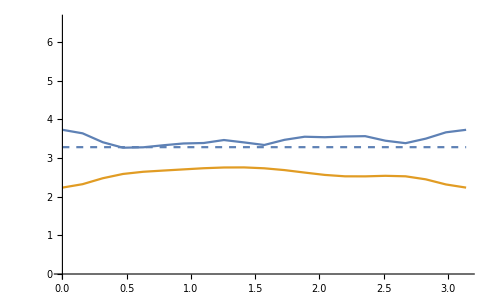

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],ListLinePlot[{tm16max,tm16mean}]]
```

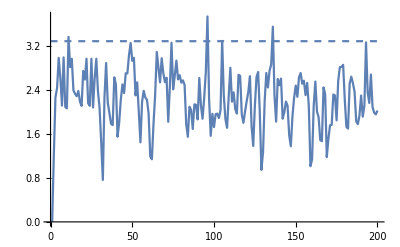

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,200},PlotStyle->Dashed],ListLinePlot[tm16n[[1]]],PlotRange->All]
```

## dt = pi/8 kick*after

#### data

```mathematica
kacorrecttmdata={-0.000000000000000000*10^+00,6.406853007629834296*10^-16,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999778*10^+00,3.999999999999997335*10^+00,3.999999999999996447*10^+00,1.999999999999999112*10^+00,1.999999999999998890*10^+00,1.281370601525966465*10^-15,1.281370601525966465*10^-15,1.281370601525966465*10^-15,1.281370601525966465*10^-15,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,3.999999999999996447*10^+00,3.999999999999995559*10^+00,3.999999999999995559*10^+00,3.999999999999994671*10^+00,1.999999999999998668*10^+00,1.999999999999998668*10^+00,3.523769154196404968*10^-15,4.164454454959387115*10^-15,1.999999999999998224*10^+00,1.999999999999998446*10^+00,1.999999999999998224*10^+00,1.999999999999998224*10^+00,3.999999999999991562*10^+00,3.999999999999991118*10^+00,1.999999999999997780*10^+00,1.999999999999997780*10^+00,3.844111804577896041*10^-15,3.844111804577896041*10^-15,3.844111804577896041*10^-15,3.844111804577896041*10^-15,1.999999999999998224*10^+00,1.999999999999998446*10^+00,3.999999999999992006*10^+00,3.999999999999991118*10^+00,1.999999999999997780*10^+00,1.999999999999998002*10^+00,1.999999999999997780*10^+00,1.999999999999997780*10^+00,5.766167706866840118*10^-15,6.406853007629821477*10^-15,6.406853007629821477*10^-15,7.047538308392801258*10^-15,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997113*10^+00,3.999999999999986233*10^+00,3.999999999999985345*10^+00,1.999999999999996669*10^+00,1.999999999999996669*10^+00,6.406853007629821477*10^-15,6.406853007629821477*10^-15,6.406853007629821477*10^-15,6.406853007629821477*10^-15,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,3.999999999999986677*10^+00,3.999999999999985789*10^+00,3.999999999999985789*10^+00,3.999999999999985345*10^+00,1.999999999999996669*10^+00,1.999999999999996669*10^+00,1.185267806411514685*10^-14,1.249336336487812427*10^-14,1.999999999999995115*10^+00,1.999999999999995337*10^+00,1.999999999999995115*10^+00,1.999999999999995115*10^+00,3.999999999999976463*10^+00,3.999999999999976019*10^+00,3.999999999999976019*10^+00,3.999999999999976907*10^+00,1.999999999999994671*10^+00,1.999999999999994671*10^+00,1.999999999999994227*10^+00,1.999999999999994227*10^+00,1.505610456793003235*10^-14,1.505610456793003235*10^-14,1.999999999999994005*10^+00,1.999999999999993783*10^+00,3.999999999999972022*10^+00,3.999999999999971578*10^+00,3.999999999999971578*10^+00,3.999999999999970690*10^+00,1.999999999999993339*10^+00,1.999999999999993339*10^+00,1.986124432365235034*10^-14,2.050192962441532775*10^-14,1.999999999999992228*10^+00,1.999999999999992006*10^+00,1.999999999999992006*10^+00,1.999999999999992450*10^+00,3.999999999999962697*10^+00,3.999999999999961808*10^+00,1.999999999999991340*10^+00,1.999999999999991340*10^+00,2.178330022594127627*10^-14,2.178330022594127627*10^-14,2.178330022594127627*10^-14,2.178330022594127627*10^-14,1.999999999999991340*10^+00,1.999999999999991562*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,3.999999999999960032*10^+00,3.999999999999959144*10^+00,3.999999999999959144*10^+00,3.999999999999958700*10^+00,1.999999999999990674*10^+00,1.999999999999990674*10^+00,2.498672672975614125*10^-14,2.562741203051911551*10^-14,1.999999999999990008*10^+00,1.999999999999990230*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,3.999999999999953815*10^+00,3.999999999999952927*10^+00,1.999999999999989342*10^+00,1.999999999999989342*10^+00,2.530706938013762680*10^-14,2.530706938013762680*10^-14,2.530706938013762680*10^-14,2.530706938013762680*10^-14,1.999999999999990008*10^+00,1.999999999999990008*10^+00,3.999999999999953815*10^+00,3.999999999999952927*10^+00,1.999999999999989564*10^+00,1.999999999999989342*10^+00,1.999999999999989342*10^+00,1.999999999999989342*10^+00,2.883083853433397103*10^-14,2.947152383509694213*10^-14,2.947152383509694213*10^-14,3.011220913585990693*10^-14,1.999999999999988454*10^+00,1.999999999999988454*10^+00,1.999999999999988232*10^+00,1.999999999999988232*10^+00,3.999999999999944489*10^+00,3.999999999999944045*10^+00,1.999999999999987788*10^+00,1.999999999999987566*10^+00,3.107323708700436989*10^-14,3.107323708700436989*10^-14,3.107323708700436989*10^-14,3.107323708700436989*10^-14,1.999999999999988010*10^+00,1.999999999999987566*10^+00,3.999999999999943601*10^+00,3.999999999999943157*10^+00,1.999999999999987566*10^+00,1.999999999999987343*10^+00,1.999999999999987343*10^+00,1.999999999999987343*10^+00,3.651906214348960534*10^-14,3.715974744425256382*10^-14,1.999999999999985789*10^+00,1.999999999999985789*10^+00,3.999999999999932943*10^+00,3.999999999999932498*10^+00,3.999999999999932498*10^+00,3.999999999999931610*10^+00,1.999999999999984901*10^+00,1.999999999999984901*10^+00,1.999999999999984901*10^+00,1.999999999999984901*10^+00,3.940214599692294375*10^-14,3.940214599692294375*10^-14,3.940214599692294375*10^-14,3.940214599692294375*10^-14,1.999999999999984679*10^+00,1.999999999999984679*10^+00,3.999999999999929390*10^+00,3.999999999999928946*10^+00,1.999999999999984013*10^+00,1.999999999999984013*10^+00,1.999999999999984013*10^+00,1.999999999999984013*10^+00,4.292591515111925958*10^-14,4.356660045188222437*10^-14,4.356660045188222437*10^-14,4.420728575264518285*10^-14,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999982681*10^+00,3.999999999999920508*10^+00,3.999999999999919620*10^+00,2.722912528242654327*10^-14,2.786981058318951437*10^-14,1.964767092222692746*10^+00,1.964767092222881706*10^+00,1.964767092222692524*10^+00,1.964767092222881706*10^+00,3.930101697794480042*10^+00,3.930101697794479598*10^+00,2.272363791976939495*10^+00,2.272363791976939051*10^+00,3.222555308971624677*10^-01,3.222555308971614685*10^-01,3.222555308971622456*10^-01,3.222555308971617460*10^-01,2.272363791976939940*10^+00,2.272363791976939940*10^+00,2.272363791976939940*10^+00,2.272363791976940384*10^+00,3.930101697794479598*10^+00,3.930101697794477822*10^+00,3.930101697794477822*10^+00,3.930101697794477822*10^+00,1.964767092222691414*10^+00,1.964767092222880596*10^+00,3.203426503814882024*10^-14,3.267495033891179134*10^-14,1.964767092222690970*10^+00,1.964767092222880152*10^+00,1.964767092222690970*10^+00,1.964767092222880152*10^+00,3.930101697794471605*10^+00,3.930101697794471161*10^+00,2.272363791976936387*10^+00,2.272363791976936387*10^+00,3.222555308971654098*10^-01,3.222555308971658539*10^-01,3.222555308971653543*10^-01,3.222555308971656318*10^-01,2.272363791976937275*10^+00,2.272363791976936831*10^+00,3.930101697794470716*10^+00,3.930101697794470716*10^+00,1.964767092222690081*10^+00,1.964767092222879485*10^+00,1.964767092222690081*10^+00,1.964767092222879263*10^+00,3.796060407020627455*10^-14,3.844111804577849972*10^-14,3.844111804577849972*10^-14,3.908180334654146451*10^-14,1.964767092222688305*10^+00,1.964767092222877931*10^+00,1.964767092222688083*10^+00,1.964767092222877487*10^+00,3.930101697794460058*10^+00,3.930101697794459614*10^+00,2.272363791976932834*10^+00,2.272363791976932834*10^+00,3.222555308971708499*10^-01,3.222555308971713495*10^-01,3.222555308971712940*10^-01,3.222555308971711829*10^-01,2.272363791976932390*10^+00,2.272363791976932390*10^+00,2.272363791976932390*10^+00,2.272363791976932390*10^+00,3.930101697794457394*10^+00,3.930101697794456506*10^+00,3.930101697794456506*10^+00,3.930101697794455617*10^+00,1.964767092222686973*10^+00,1.964767092222876377*10^+00,4.420728575264518285*10^-14,4.484797105340814765*10^-14,1.964767092222686529*10^+00,1.964767092222875711*10^+00,1.964767092222686529*10^+00,1.964767092222875711*10^+00,3.930101697794450732*10^+00,3.930101697794449844*10^+00,3.930101697794449844*10^+00,3.930101697794449844*10^+00,2.272363791976928837*10^+00,2.272363791976928837*10^+00,2.272363791976929281*10^+00,2.272363791976929281*10^+00,3.222555308971749022*10^-01,3.222555308971747356*10^-01,2.272363791976929726*10^+00,2.272363791976929281*10^+00,3.930101697794448068*10^+00,3.930101697794448512*10^+00,3.930101697794448068*10^+00,3.930101697794447624*10^+00,1.964767092222685418*10^+00,1.964767092222874600*10^+00,5.077431008546555147*10^-14,5.141499538622851626*10^-14,1.964767092222683864*10^+00,1.964767092222873490*10^+00,1.964767092222683864*10^+00,1.964767092222873490*10^+00,3.930101697794439630*10^+00,3.930101697794439186*10^+00,2.272363791976925285*10^+00,2.272363791976926173*10^+00,3.222555308971786214*10^-01,3.222555308971780108*10^-01,3.222555308971789545*10^-01,3.222555308971782329*10^-01,2.272363791976925729*10^+00,2.272363791976926173*10^+00,2.272363791976925729*10^+00,2.272363791976925729*10^+00,3.930101697794437854*10^+00,3.930101697794437410*10^+00,3.930101697794437854*10^+00,3.930101697794436078*10^+00,1.964767092222682754*10^+00,1.964767092222872380*10^+00,5.573962116637849232*10^-14,5.638030646714145081*10^-14,1.964767092222682310*10^+00,1.964767092222871714*10^+00,1.964767092222682088*10^+00,1.964767092222871270*10^+00,3.930101697794430748*10^+00,3.930101697794429860*10^+00,2.272363791976922620*10^+00,2.272363791976922176*10^+00,3.222555308971827293*10^-01,3.222555308971822297*10^-01,3.222555308971822852*10^-01,3.222555308971821741*10^-01,2.272363791976923064*10^+00,2.272363791976923508*10^+00,3.930101697794430748*10^+00,3.930101697794430748*10^+00,1.964767092222681644*10^+00,1.964767092222870826*10^+00,1.964767092222681644*10^+00,1.964767092222870826*10^+00,6.070493224729141425*10^-14,6.134561754805436011*10^-14,6.134561754805436011*10^-14,6.198630284881733121*10^-14,1.964767092222680311*10^+00,1.964767092222869493*10^+00,1.964767092222680311*10^+00,1.964767092222869493*10^+00,3.930101697794420978*10^+00,3.930101697794420978*10^+00,2.272363791976918623*10^+00,2.272363791976919956*10^+00,3.222555308971880583*10^-01,3.222555308971878363*10^-01,3.222555308971883359*10^-01,3.222555308971878363*10^-01,2.272363791976919067*10^+00,2.272363791976919956*10^+00,3.930101697794420090*10^+00,3.930101697794419202*10^+00,1.964767092222679423*10^+00,1.964767092222868605*10^+00,1.964767092222679423*10^+00,1.964767092222868605*10^+00,6.711178525492097382*10^-14,6.775247055568391968*10^-14,1.964767092222678313*10^+00,1.964767092222867717*10^+00,3.930101697794412541*10^+00,3.930101697794411653*10^+00,3.930101697794411653*10^+00,3.930101697794411209*10^+00,2.272363791976916403*10^+00,2.272363791976915959*10^+00,2.272363791976916403*10^+00,2.272363791976916403*10^+00,3.222555308971922772*10^-01,3.222555308971924437*10^-01,3.222555308971920551*10^-01,3.222555308971920551*10^-01,2.272363791976915959*10^+00,2.272363791976915515*10^+00,3.930101697794409876*10^+00,3.930101697794409432*10^+00,1.964767092222676759*10^+00,1.964767092222865941*10^+00,1.964767092222676759*10^+00,1.964767092222866385*10^+00,7.415932356331344139*10^-14,7.496018018926712687*10^-14,7.496018018926712687*10^-14,7.560086549003007273*10^-14,1.964767092222675426*10^+00,1.964767092222864608*10^+00,1.964767092222675204*10^+00,1.964767092222864608*10^+00,3.930101697794396998*10^+00,3.930101697794396998*10^+00,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,1.863352578568376217*10^+00,1.863352578568376217*10^+00,1.863352578568376217*10^+00,1.863352578568376217*10^+00,3.734969265333208277*10^+00,3.734969265333208277*10^+00,2.673377727290212391*10^+00,2.673377727290212391*10^+00,8.791435895723272997*10^-01,8.791435895723271887*10^-01,8.791435895723263005*10^-01,8.791435895723266336*10^-01,2.673377727290211503*10^+00,2.673377727290211059*10^+00,2.673377727290210615*10^+00,2.673377727290211059*10^+00,3.734969265333205168*10^+00,3.734969265333204724*10^+00,3.734969265333205168*10^+00,3.734969265333204724*10^+00,1.863352578568375328*10^+00,1.863352578568375328*10^+00,5.926339032057585260*10^-15,6.727195658011310973*10^-15,1.863352578568374440*10^+00,1.863352578568374440*10^+00,1.863352578568373996*10^+00,1.863352578568374440*10^+00,3.734969265333197619*10^+00,3.734969265333198063*10^+00,2.673377727290205730*10^+00,2.673377727290206174*10^+00,8.791435895723291871*10^-01,8.791435895723289651*10^-01,8.791435895723289651*10^-01,8.791435895723287430*10^-01,2.673377727290206174*10^+00,2.673377727290206618*10^+00,3.734969265333197619*10^+00,3.734969265333198507*10^+00,1.863352578568374218*10^+00,1.863352578568374218*10^+00,1.863352578568373996*10^+00,1.863352578568373996*10^+00,1.073147878777993322*10^-14,1.153233541373365815*10^-14,1.153233541373365815*10^-14,1.217302071449663556*10^-14,1.863352578568372664*10^+00,1.863352578568373108*10^+00,1.863352578568372886*10^+00,1.863352578568372886*10^+00,3.734969265333190069*10^+00,3.734969265333190069*10^+00,2.673377727290200845*10^+00,2.673377727290202177*10^+00,8.791435895723307414*10^-01,8.791435895723297422*10^-01,8.791435895723301863*10^-01,8.791435895723302973*10^-01,2.673377727290201733*10^+00,2.673377727290202177*10^+00,2.673377727290201289*10^+00,2.673377727290200845*10^+00,3.734969265333189181*10^+00,3.734969265333188737*10^+00,3.734969265333189181*10^+00,3.734969265333188293*10^+00,1.863352578568372442*10^+00,1.863352578568372220*10^+00,1.697816047021896459*10^-14,1.745867444579119608*10^-14,1.863352578568371332*10^+00,1.863352578568371332*10^+00,1.863352578568371332*10^+00,1.863352578568371332*10^+00,3.734969265333180743*10^+00,3.734969265333180743*10^+00,3.734969265333180299*10^+00,3.734969265333180743*10^+00,2.673377727290196848*10^+00,2.673377727290196848*10^+00,2.673377727290195516*10^+00,2.673377727290195516*10^+00,8.791435895723327398*10^-01,8.791435895723324068*10^-01,2.673377727290196404*10^+00,2.673377727290195960*10^+00,3.734969265333179411*10^+00,3.734969265333178079*10^+00,3.734969265333178523*10^+00,3.734969265333178079*10^+00,1.863352578568370443*10^+00,1.863352578568370443*10^+00,2.290449950227647886*10^-14,2.338501347784871034*10^-14,1.863352578568369777*10^+00,1.863352578568369777*10^+00,1.863352578568369999*10^+00,1.863352578568369999*10^+00,3.734969265333173194*10^+00,3.734969265333172306*10^+00,2.673377727290191075*10^+00,2.673377727290192851*10^+00,8.791435895723340721*10^-01,8.791435895723336280*10^-01,8.791435895723334060*10^-01,8.791435895723334060*10^-01,2.673377727290191519*10^+00,2.673377727290191963*10^+00,2.673377727290191519*10^+00,2.673377727290191519*10^+00,3.734969265333171862*10^+00,3.734969265333171418*10^+00,3.734969265333171862*10^+00,3.734969265333171418*10^+00,1.863352578568369555*10^+00,1.863352578568369333*10^+00,2.835032455876174270*10^-14,2.883083853433397103*10^-14,1.863352578568368223*10^+00,1.863352578568368223*10^+00,1.863352578568368223*10^+00,1.863352578568368223*10^+00,3.734969265333163868*10^+00,3.734969265333163424*10^+00,2.673377727290186634*10^+00,2.673377727290187078*10^+00,8.791435895723374028*10^-01,8.791435895723370697*10^-01,8.791435895723370697*10^-01,8.791435895723371807*10^-01,2.673377727290186634*10^+00,2.673377727290185746*10^+00,3.734969265333162536*10^+00,3.734969265333162092*10^+00,1.863352578568367557*10^+00,1.863352578568367557*10^+00,1.863352578568367335*10^+00,1.863352578568367335*10^+00,3.507752021677292351*10^-14,3.587837684272663424*10^-14,3.603854816791737386*10^-14,3.651906214348960534*10^-14,1.863352578568366003*10^+00,1.863352578568366003*10^+00,1.863352578568366003*10^+00,1.863352578568365780*10^+00,3.734969265333151878*10^+00,3.734969265333151434*10^+00,2.673377727290180417*10^+00,2.673377727290180861*10^+00,8.791435895723402894*10^-01,8.791435895723400673*10^-01,8.791435895723399563*10^-01,8.791435895723396232*10^-01,2.673377727290179973*10^+00,2.673377727290180417*10^+00,3.734969265333150545*10^+00,3.734969265333149213*10^+00,1.863352578568365114*10^+00,1.863352578568365114*10^+00,1.863352578568365114*10^+00,1.863352578568365114*10^+00,4.212505852516554885*10^-14,4.276574382592851365*10^-14,1.863352578568364226*10^+00,1.863352578568363782*10^+00,3.734969265333141664*10^+00,3.734969265333140775*10^+00,3.734969265333141664*10^+00,3.734969265333141220*10^+00,2.673377727290176420*10^+00,2.673377727290175532*10^+00,2.673377727290174199*10^+00,2.673377727290175976*10^+00,8.791435895723413996*10^-01,8.791435895723413996*10^-01,8.791435895723411775*10^-01,8.791435895723406224*10^-01,2.673377727290175088*10^+00,2.673377727290174644*10^+00,3.734969265333140775*10^+00,3.734969265333139887*10^+00,1.863352578568363782*10^+00,1.863352578568363782*10^+00,1.863352578568363782*10^+00,1.863352578568363782*10^+00,4.789122623203222568*10^-14,4.853191153279518416*10^-14,4.837174020760444454*10^-14,4.917259683355814264*10^-14,1.863352578568362450*10^+00,1.863352578568362006*10^+00,1.863352578568362006*10^+00,1.863352578568362006*10^+00,3.734969265333132338*10^+00,3.734969265333132338*10^+00,9.610279511444749964*10^-16,1.761884577098203667*10^-15,1.707978246994109162*10^+00,1.707978246994108940*10^+00,1.707978246994109162*10^+00,1.707978246994108940*10^+00,3.451690335526873099*10^+00,3.451690335526872211*10^+00,2.978836514958032922*10^+00,2.978836514958032478*10^+00,1.381077963249261575*10^+00,1.381077963249261353*10^+00,1.381077963249261575*10^+00,1.381077963249261353*10^+00,2.978836514958030701*10^+00,2.978836514958032033*10^+00,2.978836514958030701*10^+00,2.978836514958031589*10^+00,3.451690335526870435*10^+00,3.451690335526869990*10^+00,3.451690335526869990*10^+00,3.451690335526869546*10^+00,1.707978246994108940*10^+00,1.707978246994108718*10^+00,7.528052283965036685*10^-15,8.008566259537272901*10^-15,1.707978246994107607*10^+00,1.707978246994107829*10^+00,1.707978246994108273*10^+00,1.707978246994107385*10^+00,3.451690335526862441*10^+00,3.451690335526861997*10^+00,2.978836514958024928*10^+00,2.978836514958024484*10^+00,1.381077963249262464*10^+00,1.381077963249262908*10^+00,1.381077963249262908*10^+00,1.381077963249262908*10^+00,2.978836514958024040*10^+00,2.978836514958024484*10^+00,3.451690335526859776*10^+00,3.451690335526860220*10^+00,1.707978246994107607*10^+00,1.707978246994107607*10^+00,1.707978246994107385*10^+00,1.707978246994107607*10^+00,1.409507661678556938*10^-14,1.473576191754854364*10^-14,1.505610456793003235*10^-14,1.553661854350226699*10^-14,1.707978246994106497*10^+00,1.707978246994106497*10^+00,1.707978246994106275*10^+00,1.707978246994106275*10^+00,3.451690335526853115*10^+00,3.451690335526852671*10^+00,2.978836514958017823*10^+00,2.978836514958017823*10^+00,1.381077963249263352*10^+00,1.381077963249263130*10^+00,1.381077963249263130*10^+00,1.381077963249262908*10^+00,2.978836514958016934*10^+00,2.978836514958015602*10^+00,2.978836514958016046*10^+00,2.978836514958016490*10^+00,3.451690335526849118*10^+00,3.451690335526849118*10^+00,3.451690335526848674*10^+00,3.451690335526849118*10^+00,1.707978246994105831*10^+00,1.707978246994105831*10^+00,2.162312890075053034*10^-14,2.194347155113201904*10^-14,1.707978246994105387*10^+00,1.707978246994105165*10^+00,1.707978246994105387*10^+00,1.707978246994105165*10^+00,3.451690335526844677*10^+00,3.451690335526843789*10^+00,3.451690335526843345*10^+00,3.451690335526843345*10^+00,2.978836514958010273*10^+00,2.978836514958009829*10^+00,2.978836514958010273*10^+00,2.978836514958010273*10^+00,1.381077963249263130*10^+00,1.381077963249262464*10^+00,2.978836514958010273*10^+00,2.978836514958008941*10^+00,3.451690335526841125*10^+00,3.451690335526840681*10^+00,3.451690335526841125*10^+00,3.451690335526840681*10^+00,1.707978246994104721*10^+00,1.707978246994104943*10^+00,2.786981058318951437*10^-14,2.802998190838025715*10^-14,1.707978246994104277*10^+00,1.707978246994104277*10^+00,1.707978246994104277*10^+00,1.707978246994104055*10^+00,3.451690335526835351*10^+00,3.451690335526835796*10^+00,2.978836514958004500*10^+00,2.978836514958003168*10^+00,1.381077963249264240*10^+00,1.381077963249263574*10^+00,1.381077963249263574*10^+00,1.381077963249263352*10^+00,2.978836514958001835*10^+00,2.978836514958002724*10^+00,2.978836514958002724*10^+00,2.978836514958001835*10^+00,3.451690335526833131*10^+00,3.451690335526830911*10^+00,3.451690335526832243*10^+00,3.451690335526831355*10^+00,1.707978246994103833*10^+00,1.707978246994103610*10^+00,3.379614961524698762*10^-14,3.427666359081921279*10^-14,1.707978246994103166*10^+00,1.707978246994103166*10^+00,1.707978246994102944*10^+00,1.707978246994103166*10^+00,3.451690335526827358*10^+00,3.451690335526826470*10^+00,2.978836514957996506*10^+00,2.978836514957996950*10^+00,1.381077963249263352*10^+00,1.381077963249263352*10^+00,1.381077963249263130*10^+00,1.381077963249262686*10^+00,2.978836514957995174*10^+00,2.978836514957996062*10^+00,3.451690335526825137*10^+00,3.451690335526824693*10^+00,1.707978246994102722*10^+00,1.707978246994102944*10^+00,1.707978246994102944*10^+00,1.707978246994102722*10^+00,4.020300262287665448*10^-14,4.084368792363962558*10^-14,4.068351659844887965*10^-14,4.148437322440259037*10^-14,1.707978246994101834*10^+00,1.707978246994102278*10^+00,1.707978246994101834*10^+00,1.707978246994101834*10^+00,3.451690335526816700*10^+00,3.451690335526817144*10^+00,2.978836514957988957*10^+00,2.978836514957989401*10^+00,1.381077963249264240*10^+00,1.381077963249264018*10^+00,1.381077963249264240*10^+00,1.381077963249264240*10^+00,2.978836514957988069*10^+00,2.978836514957988069*10^+00,3.451690335526813591*10^+00,3.451690335526813591*10^+00,1.707978246994100946*10^+00,1.707978246994101390*10^+00,1.707978246994101390*10^+00,1.707978246994101168*10^+00,4.741071225646000051*10^-14,4.821156888241370492*10^-14,1.707978246994100502*10^+00,1.707978246994100502*10^+00,3.451690335526808262*10^+00,3.451690335526807818*10^+00,3.451690335526807818*10^+00,3.451690335526806042*10^+00,2.978836514957981851*10^+00,2.978836514957981851*10^+00,2.978836514957981407*10^+00,2.978836514957981407*10^+00,1.381077963249264684*10^+00,1.381077963249264462*10^+00,1.381077963249264684*10^+00,1.381077963249264018*10^+00,2.978836514957980963*10^+00,2.978836514957980519*10^+00,3.451690335526805598*10^+00,3.451690335526802933*10^+00,1.707978246994100280*10^+00,1.707978246994100058*10^+00,1.707978246994100058*10^+00,1.707978246994100058*10^+00,5.397773658928035019*10^-14,5.477859321523404829*10^-14,5.477859321523404829*10^-14,5.573962116637849232*10^-14,1.707978246994099170*10^+00,1.707978246994099392*10^+00,1.707978246994099170*10^+00,1.707978246994099170*10^+00,3.451690335526797160*10^+00,3.451690335526796272*10^+00,4.805139755722374982*10^-16,1.281370601525966465*10^-15,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024021096*10^+00,1.516990580024020874*10^+00,3.124515482622840956*10^+00,3.124515482622841844*10^+00,3.079451268076446091*10^+00,3.079451268076446091*10^+00,1.724922032546203798*10^+00,1.724922032546203798*10^+00,1.724922032546203798*10^+00,1.724922032546203798*10^+00,3.079451268076444759*10^+00,3.079451268076445647*10^+00,3.079451268076445203*10^+00,3.079451268076445203*10^+00,3.124515482622838736*10^+00,3.124515482622839180*10^+00,3.124515482622838736*10^+00,3.124515482622838736*10^+00,1.516990580024021096*10^+00,1.516990580024020874*10^+00,7.367880958774292331*10^-15,8.008566259537272901*10^-15,1.516990580024020652*10^+00,1.516990580024020430*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,3.124515482622834739*10^+00,3.124515482622832518*10^+00,3.079451268076439874*10^+00,3.079451268076439874*10^+00,1.724922032546202466*10^+00,1.724922032546202466*10^+00,1.724922032546202022*10^+00,1.724922032546202022*10^+00,3.079451268076438097*10^+00,3.079451268076439430*10^+00,3.124515482622832074*10^+00,3.124515482622832074*10^+00,1.516990580024021096*10^+00,1.516990580024021096*10^+00,1.516990580024021096*10^+00,1.516990580024020874*10^+00,1.329421999083184604*10^-14,1.409507661678556938*10^-14,1.377473396640408068*10^-14,1.473576191754854364*10^-14,1.516990580024020652*10^+00,1.516990580024020874*10^+00,1.516990580024020430*10^+00,1.516990580024020874*10^+00,3.124515482622828522*10^+00,3.124515482622827633*10^+00,3.079451268076432324*10^+00,3.079451268076431436*10^+00,1.724922032546200690*10^+00,1.724922032546200690*10^+00,1.724922032546200690*10^+00,1.724922032546200468*10^+00,3.079451268076430548*10^+00,3.079451268076430992*10^+00,3.079451268076430104*10^+00,3.079451268076430548*10^+00,3.124515482622824969*10^+00,3.124515482622824081*10^+00,3.124515482622823637*10^+00,3.124515482622824525*10^+00,1.516990580024020874*10^+00,1.516990580024020874*10^+00,2.050192962441532775*10^-14,2.098244359998755608*10^-14,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,3.124515482622820528*10^+00,3.124515482622820528*10^+00,3.124515482622820528*10^+00,3.124515482622818752*10^+00,3.079451268076423887*10^+00,3.079451268076423887*10^+00,3.079451268076423887*10^+00,3.079451268076423442*10^+00,1.724922032546198913*10^+00,1.724922032546199357*10^+00,3.079451268076423442*10^+00,3.079451268076423442*10^+00,3.124515482622817864*10^+00,3.124515482622818752*10^+00,3.124515482622817864*10^+00,3.124515482622817864*10^+00,1.516990580024021096*10^+00,1.516990580024020652*10^+00,2.722912528242654327*10^-14,2.770963925799877160*10^-14,1.516990580024020430*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020208*10^+00,3.124515482622813423*10^+00,3.124515482622813423*10^+00,3.079451268076416781*10^+00,3.079451268076417225*10^+00,1.724922032546197581*10^+00,1.724922032546197137*10^+00,1.724922032546197581*10^+00,1.724922032546197359*10^+00,3.079451268076416781*10^+00,3.079451268076416337*10^+00,3.079451268076416337*10^+00,3.079451268076415005*10^+00,3.124515482622810758*10^+00,3.124515482622810758*10^+00,3.124515482622810758*10^+00,3.124515482622810758*10^+00,1.516990580024020430*10^+00,1.516990580024020652*10^+00,3.299529298929327058*10^-14,3.379614961524698762*10^-14,1.516990580024020208*10^+00,1.516990580024020430*10^+00,1.516990580024020430*10^+00,1.516990580024020430*10^+00,3.124515482622807649*10^+00,3.124515482622805873*10^+00,3.079451268076409232*10^+00,3.079451268076409232*10^+00,1.724922032546196249*10^+00,1.724922032546195805*10^+00,1.724922032546195805*10^+00,1.724922032546195805*10^+00,3.079451268076409232*10^+00,3.079451268076408343*10^+00,3.124515482622804541*10^+00,3.124515482622803653*10^+00,1.516990580024020430*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020430*10^+00,3.812077539539701417*10^-14,3.876146069615998527*10^-14,3.876146069615998527*10^-14,3.940214599692294375*10^-14,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020874*10^+00,1.516990580024020874*10^+00,3.124515482622800988*10^+00,3.124515482622800100*10^+00,3.079451268076403014*10^+00,3.079451268076402570*10^+00,1.724922032546194250*10^+00,1.724922032546194028*10^+00,1.724922032546194250*10^+00,1.724922032546194250*10^+00,3.079451268076402126*10^+00,3.079451268076402570*10^+00,3.124515482622800100*10^+00,3.124515482622798768*10^+00,1.516990580024021096*10^+00,1.516990580024021318*10^+00,1.516990580024020874*10^+00,1.516990580024020874*10^+00,4.484797105340814765*10^-14,4.548865635417111875*10^-14,1.516990580024020652*10^+00,1.516990580024021096*10^+00,3.124515482622794771*10^+00,3.124515482622792995*10^+00,3.124515482622793883*10^+00,3.124515482622793439*10^+00,3.079451268076395909*10^+00,3.079451268076396797*10^+00,3.079451268076396797*10^+00,3.079451268076395021*10^+00,1.724922032546192696*10^+00,1.724922032546192696*10^+00,1.724922032546192696*10^+00,1.724922032546192474*10^+00,3.079451268076394133*10^+00,3.079451268076393688*10^+00,3.124515482622792106*10^+00,3.124515482622791662*10^+00,1.516990580024021096*10^+00,1.516990580024020874*10^+00,1.516990580024020874*10^+00,1.516990580024021096*10^+00,5.077431008546555147*10^-14,5.125482406103777033*10^-14,5.125482406103777033*10^-14,5.189550936180072881*10^-14,1.516990580024021096*10^+00,1.516990580024021096*10^+00,1.516990580024021318*10^+00,1.516990580024020874*10^+00,3.124515482622788554*10^+00,3.124515482622787665*10^+00,3.203426503814917641*10^-16,3.203426503814917641*10^-16,1.312115125945429339*10^+00,1.312115125945429783*10^+00,1.312115125945429783*10^+00,1.312115125945429561*10^+00,2.790914008573441851*10^+00,2.790914008573441407*10^+00,3.025317756887095921*10^+00,3.025317756887095477*10^+00,1.900222886831056890*10^+00,1.900222886831056890*10^+00,1.900222886831056890*10^+00,1.900222886831056446*10^+00,3.025317756887094589*10^+00,3.025317756887094145*10^+00,3.025317756887093701*10^+00,3.025317756887094145*10^+00,2.790914008573438743*10^+00,2.790914008573438743*10^+00,2.790914008573438743*10^+00,2.790914008573438743*10^+00,1.312115125945430227*10^+00,1.312115125945430449*10^+00,6.887366983202056115*10^-15,7.367880958774292331*10^-15,1.312115125945430449*10^+00,1.312115125945430671*10^+00,1.312115125945430227*10^+00,1.312115125945430893*10^+00,2.790914008573435634*10^+00,2.790914008573435634*10^+00,3.025317756887089260*10^+00,3.025317756887089260*10^+00,1.900222886831054447*10^+00,1.900222886831054447*10^+00,1.900222886831054447*10^+00,1.900222886831054447*10^+00,3.025317756887086595*10^+00,3.025317756887087484*10^+00,2.790914008573432969*10^+00,2.790914008573432081*10^+00,1.312115125945430893*10^+00,1.312115125945431560*10^+00,1.312115125945430893*10^+00,1.312115125945431338*10^+00,1.409507661678556938*10^-14,1.473576191754854364*10^-14,1.457559059235780087*10^-14,1.521627589312077828*10^-14,1.312115125945431560*10^+00,1.312115125945431338*10^+00,1.312115125945431560*10^+00,1.312115125945431338*10^+00,2.790914008573428085*10^+00,2.790914008573428973*10^+00,3.025317756887079046*10^+00,3.025317756887079490*10^+00,1.900222886831052227*10^+00,1.900222886831052005*10^+00,1.900222886831052005*10^+00,1.900222886831052005*10^+00,3.025317756887079046*10^+00,3.025317756887079490*10^+00,3.025317756887078158*10^+00,3.025317756887079490*10^+00,2.790914008573427640*10^+00,2.790914008573424976*10^+00,2.790914008573427196*10^+00,2.790914008573425420*10^+00,1.312115125945432226*10^+00,1.312115125945432004*10^+00,2.146295757555979072*10^-14,2.210364287632276498*10^-14,1.312115125945432448*10^+00,1.312115125945432448*10^+00,1.312115125945432670*10^+00,1.312115125945432448*10^+00,2.790914008573422755*10^+00,2.790914008573421867*10^+00,2.790914008573421867*10^+00,2.790914008573423200*10^+00,3.025317756887073273*10^+00,3.025317756887072385*10^+00,3.025317756887071940*10^+00,3.025317756887072385*10^+00,1.900222886831049562*10^+00,1.900222886831049562*10^+00,3.025317756887071052*10^+00,3.025317756887071052*10^+00,2.790914008573421867*10^+00,2.790914008573419203*10^+00,2.790914008573420979*10^+00,2.790914008573420535*10^+00,1.312115125945432892*10^+00,1.312115125945433114*10^+00,2.883083853433397103*10^-14,2.915118118471545658*10^-14,1.312115125945433114*10^+00,1.312115125945433558*10^+00,1.312115125945433114*10^+00,1.312115125945433114*10^+00,2.790914008573416538*10^+00,2.790914008573415650*10^+00,3.025317756887065723*10^+00,3.025317756887065279*10^+00,1.900222886831047564*10^+00,1.900222886831047342*10^+00,1.900222886831047342*10^+00,1.900222886831047120*10^+00,3.025317756887063947*10^+00,3.025317756887064391*10^+00,3.025317756887063059*10^+00,3.025317756887063503*10^+00,2.790914008573413430*10^+00,2.790914008573414318*10^+00,2.790914008573413430*10^+00,2.790914008573413430*10^+00,1.312115125945434002*10^+00,1.312115125945434002*10^+00,3.619871949310811348*10^-14,3.683940479387108458*10^-14,1.312115125945434446*10^+00,1.312115125945434446*10^+00,1.312115125945434224*10^+00,1.312115125945434224*10^+00,2.790914008573410765*10^+00,2.790914008573410765*10^+00,3.025317756887056397*10^+00,3.025317756887056397*10^+00,1.900222886831045122*10^+00,1.900222886831045122*10^+00,1.900222886831045344*10^+00,1.900222886831044899*10^+00,3.025317756887056397*10^+00,3.025317756887056397*10^+00,2.790914008573408100*10^+00,2.790914008573408545*10^+00,1.312115125945434890*10^+00,1.312115125945435112*10^+00,1.312115125945434890*10^+00,1.312115125945434890*10^+00,4.244540117554703441*10^-14,4.324625780150074513*10^-14,4.308608647630999920*10^-14,4.356660045188222437*10^-14,1.312115125945435778*10^+00,1.312115125945435334*10^+00,1.312115125945435556*10^+00,1.312115125945435556*10^+00,2.790914008573405436*10^+00,2.790914008573404548*10^+00,3.025317756887051068*10^+00,3.025317756887050624*10^+00,1.900222886831043123*10^+00,1.900222886831042901*10^+00,1.900222886831042901*10^+00,1.900222886831042679*10^+00,3.025317756887047516*10^+00,3.025317756887047960*10^+00,2.790914008573402327*10^+00,2.790914008573402771*10^+00,1.312115125945435778*10^+00,1.312115125945436223*10^+00,1.312115125945435778*10^+00,1.312115125945435778*10^+00,4.997345345951185337*10^-14,5.061413876027481185*10^-14,1.312115125945436223*10^+00,1.312115125945436001*10^+00,2.790914008573400107*10^+00,2.790914008573398775*10^+00,2.790914008573397886*10^+00,2.790914008573398331*10^+00,3.025317756887042631*10^+00,3.025317756887043075*10^+00,3.025317756887042631*10^+00,3.025317756887042187*10^+00,1.900222886831040903*10^+00,1.900222886831040459*10^+00,1.900222886831040459*10^+00,1.900222886831040459*10^+00,3.025317756887040854*10^+00,3.025317756887040410*10^+00,2.790914008573396110*10^+00,2.790914008573395222*10^+00,1.312115125945436889*10^+00,1.312115125945436667*10^+00,1.312115125945436445*10^+00,1.312115125945436667*10^+00,5.702099176790440298*10^-14,5.750150574347662184*10^-14,5.734133441828588222*10^-14,5.798201971904884070*10^-14,1.312115125945437111*10^+00,1.312115125945436889*10^+00,1.312115125945437111*10^+00,1.312115125945436667*10^+00,2.790914008573392557*10^+00,2.790914008573392113*10^+00,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,1.115222582521595118*10^+00,1.115222582521596006*10^+00,1.115222582521596006*10^+00,1.115222582521595562*10^+00,2.455030932036220470*10^+00,2.455030932036220026*10^+00,2.866494150121563944*10^+00,2.866494150121563944*10^+00,1.950012215869782572*10^+00,1.950012215869782572*10^+00,1.950012215869782350*10^+00,1.950012215869782350*10^+00,2.866494150121563944*10^+00,2.866494150121563500*10^+00,2.866494150121562612*10^+00,2.866494150121561724*10^+00,2.455030932036219138*10^+00,2.455030932036218250*10^+00,2.455030932036218250*10^+00,2.455030932036218250*10^+00,1.115222582521597339*10^+00,1.115222582521597117*10^+00,5.926339032057585260*10^-15,7.047538308392801258*10^-15,1.115222582521598227*10^+00,1.115222582521597783*10^+00,1.115222582521598227*10^+00,1.115222582521597783*10^+00,2.455030932036216917*10^+00,2.455030932036216917*10^+00,2.866494150121556839*10^+00,2.866494150121557283*10^+00,1.950012215869780130*10^+00,1.950012215869780130*10^+00,1.950012215869780130*10^+00,1.950012215869779908*10^+00,2.866494150121557727*10^+00,2.866494150121555506*10^+00,2.455030932036214697*10^+00,2.455030932036214253*10^+00,1.115222582521599559*10^+00,1.115222582521598893*10^+00,1.115222582521599337*10^+00,1.115222582521599559*10^+00,1.281370601525961455*10^-14,1.345439131602259039*10^-14,1.329421999083184604*10^-14,1.409507661678556938*10^-14,1.115222582521600225*10^+00,1.115222582521600225*10^+00,1.115222582521600447*10^+00,1.115222582521600003*10^+00,2.455030932036213365*10^+00,2.455030932036211588*10^+00,2.866494150121551510*10^+00,2.866494150121551954*10^+00,1.950012215869777243*10^+00,1.950012215869777243*10^+00,1.950012215869777465*10^+00,1.950012215869777243*10^+00,2.866494150121548845*10^+00,2.866494150121549289*10^+00,2.866494150121548401*10^+00,2.866494150121549289*10^+00,2.455030932036210256*10^+00,2.455030932036209812*10^+00,2.455030932036209812*10^+00,2.455030932036209812*10^+00,1.115222582521601780*10^+00,1.115222582521601558*10^+00,2.098244359998755608*10^-14,2.114261492517830201*10^-14,1.115222582521602668*10^+00,1.115222582521602446*10^+00,1.115222582521602446*10^+00,1.115222582521602224*10^+00,2.455030932036207592*10^+00,2.455030932036208036*10^+00,2.455030932036206703*10^+00,2.455030932036207147*10^+00,2.866494150121543960*10^+00,2.866494150121544404*10^+00,2.866494150121543960*10^+00,2.866494150121543960*10^+00,1.950012215869775023*10^+00,1.950012215869775023*10^+00,2.866494150121543072*10^+00,2.866494150121542628*10^+00,2.455030932036205815*10^+00,2.455030932036205371*10^+00,2.455030932036205815*10^+00,2.455030932036204483*10^+00,1.115222582521604000*10^+00,1.115222582521603778*10^+00,2.819015323357099993*10^-14,2.851049588395248548*10^-14,1.115222582521604444*10^+00,1.115222582521604444*10^+00,1.115222582521604666*10^+00,1.115222582521604888*10^+00,2.455030932036202262*10^+00,2.455030932036202707*10^+00,2.866494150121538187*10^+00,2.866494150121537743*10^+00,1.950012215869772358*10^+00,1.950012215869772358*10^+00,1.950012215869772358*10^+00,1.950012215869772358*10^+00,2.866494150121536411*10^+00,2.866494150121537299*10^+00,2.866494150121535522*10^+00,2.866494150121535522*10^+00,2.455030932036200042*10^+00,2.455030932036200486*10^+00,2.455030932036200042*10^+00,2.455030932036200042*10^+00,1.115222582521605776*10^+00,1.115222582521605776*10^+00,3.587837684272663424*10^-14,3.619871949310811348*10^-14,1.115222582521606443*10^+00,1.115222582521606443*10^+00,1.115222582521606665*10^+00,1.115222582521606443*10^+00,2.455030932036198266*10^+00,2.455030932036197377*10^+00,2.866494150121531526*10^+00,2.866494150121530637*10^+00,1.950012215869769916*10^+00,1.950012215869769916*10^+00,1.950012215869769916*10^+00,1.950012215869769694*10^+00,2.866494150121529305*10^+00,2.866494150121528861*10^+00,2.455030932036196489*10^+00,2.455030932036196045*10^+00,1.115222582521608219*10^+00,1.115222582521607997*10^+00,1.115222582521607997*10^+00,1.115222582521607775*10^+00,4.292591515111925958*10^-14,4.324625780150074513*10^-14,4.340642912669147844*10^-14,4.388694310226370361*10^-14,1.115222582521608885*10^+00,1.115222582521608885*10^+00,1.115222582521608663*10^+00,1.115222582521608219*10^+00,2.455030932036192937*10^+00,2.455030932036192493*10^+00,2.866494150121523088*10^+00,2.866494150121523532*10^+00,1.950012215869767251*10^+00,1.950012215869767251*10^+00,1.950012215869767251*10^+00,1.950012215869767029*10^+00,2.866494150121522200*10^+00,2.866494150121522200*10^+00,2.455030932036191160*10^+00,2.455030932036191160*10^+00,1.115222582521610217*10^+00,1.115222582521610217*10^+00,1.115222582521610217*10^+00,1.115222582521609773*10^+00,5.061413876027481185*10^-14,5.077431008546555147*10^-14,1.115222582521610883*10^+00,1.115222582521610661*10^+00,2.455030932036188940*10^+00,2.455030932036188940*10^+00,2.455030932036188496*10^+00,2.455030932036188052*10^+00,2.866494150121516427*10^+00,2.866494150121517759*10^+00,2.866494150121517759*10^+00,2.866494150121516871*10^+00,1.950012215869764365*10^+00,1.950012215869764809*10^+00,1.950012215869764365*10^+00,1.950012215869764365*10^+00,2.866494150121515094*10^+00,2.866494150121515982*10^+00,2.455030932036185831*10^+00,2.455030932036185831*10^+00,1.115222582521612438*10^+00,1.115222582521612216*10^+00,1.115222582521612216*10^+00,1.115222582521611772*10^+00,5.830236236943031994*10^-14,5.862270501981179918*10^-14,5.894304767019327842*10^-14,5.958373297095623690*10^-14,1.115222582521612882*10^+00,1.115222582521612882*10^+00,1.115222582521612882*10^+00,1.115222582521613326*10^+00,2.455030932036183167*10^+00,2.455030932036183167*10^+00,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,9.452589891428949676*10^-01,9.452589891428948565*10^-01,9.452589891428943014*10^-01,9.452589891428950786*10^-01,2.192514343801554855*10^+00,2.192514343801555743*10^+00,2.647555843618305094*10^+00,2.647555843618304650*10^+00,1.928206233734424124*10^+00,1.928206233734423680*10^+00,1.928206233734423680*10^+00,1.928206233734423680*10^+00,2.647555843618303317*10^+00,2.647555843618302429*10^+00,2.647555843618302873*10^+00,2.647555843618303317*10^+00,2.192514343801553522*10^+00,2.192514343801552634*10^+00,2.192514343801553522*10^+00,2.192514343801553522*10^+00,9.452589891428967439*10^-01,9.452589891428967439*10^-01,7.688223609155782616*10^-15,8.328908909918763186*10^-15,9.452589891428979652*10^-01,9.452589891428977431*10^-01,9.452589891428977431*10^-01,9.452589891428979652*10^-01,2.192514343801551746*10^+00,2.192514343801551746*10^+00,2.647555843618299320*10^+00,2.647555843618297988*10^+00,1.928206233734421016*10^+00,1.928206233734421016*10^+00,1.928206233734421016*10^+00,1.928206233734421016*10^+00,2.647555843618297100*10^+00,2.647555843618297100*10^+00,2.192514343801550858*10^+00,2.192514343801549970*10^+00,9.452589891428998525*10^-01,9.452589891428995195*10^-01,9.452589891429000746*10^-01,9.452589891428998525*10^-01,1.521627589312077828*10^-14,1.633747516945598718*10^-14,1.633747516945598718*10^-14,1.665781781983747589*10^-14,9.452589891429011848*10^-01,9.452589891429010738*10^-01,9.452589891429014068*10^-01,9.452589891429012958*10^-01,2.192514343801548193*10^+00,2.192514343801547749*10^+00,2.647555843618293103*10^+00,2.647555843618292215*10^+00,1.928206233734418795*10^+00,1.928206233734418795*10^+00,1.928206233734418351*10^+00,1.928206233734418351*10^+00,2.647555843618290439*10^+00,2.647555843618290439*10^+00,2.647555843618290439*10^+00,2.647555843618290439*10^+00,2.192514343801546417*10^+00,2.192514343801545973*10^+00,2.192514343801545529*10^+00,2.192514343801545529*10^+00,9.452589891429034052*10^-01,9.452589891429032942*10^-01,2.498672672975614125*10^-14,2.498672672975614125*10^-14,9.452589891429044044*10^-01,9.452589891429046265*10^-01,9.452589891429045155*10^-01,9.452589891429045155*10^-01,2.192514343801544641*10^+00,2.192514343801544641*10^+00,2.192514343801543308*10^+00,2.192514343801543308*10^+00,2.647555843618285110*10^+00,2.647555843618285998*10^+00,2.647555843618284666*10^+00,2.647555843618285110*10^+00,1.928206233734416131*10^+00,1.928206233734415687*10^+00,2.647555843618283333*10^+00,2.647555843618283777*10^+00,2.192514343801541532*10^+00,2.192514343801541532*10^+00,2.192514343801541976*10^+00,2.192514343801541088*10^+00,9.452589891429068469*10^-01,9.452589891429068469*10^-01,3.347580696486550206*10^-14,3.331563563967475613*10^-14,9.452589891429079572*10^-01,9.452589891429075131*10^-01,9.452589891429075131*10^-01,9.452589891429078461*10^-01,2.192514343801539756*10^+00,2.192514343801540200*10^+00,2.647555843618278892*10^+00,2.647555843618278892*10^+00,1.928206233734413466*10^+00,1.928206233734413022*10^+00,1.928206233734413466*10^+00,1.928206233734413022*10^+00,2.647555843618277560*10^+00,2.647555843618277560*10^+00,2.647555843618278004*10^+00,2.647555843618277116*10^+00,2.192514343801537535*10^+00,2.192514343801537535*10^+00,2.192514343801537979*10^+00,2.192514343801537535*10^+00,9.452589891429096225*10^-01,9.452589891429099556*10^-01,4.100385924883035889*10^-14,4.164454454959332999*10^-14,9.452589891429108437*10^-01,9.452589891429107327*10^-01,9.452589891429110658*10^-01,9.452589891429112878*10^-01,2.192514343801535759*10^+00,2.192514343801535759*10^+00,2.647555843618273119*10^+00,2.647555843618272231*10^+00,1.928206233734410802*10^+00,1.928206233734410580*10^+00,1.928206233734410802*10^+00,1.928206233734410580*10^+00,2.647555843618270899*10^+00,2.647555843618271343*10^+00,2.192514343801534427*10^+00,2.192514343801533983*10^+00,9.452589891429126201*10^-01,9.452589891429127311*10^-01,9.452589891429130642*10^-01,9.452589891429131752*10^-01,4.933276815874888857*10^-14,4.965311080913036781*10^-14,4.981328213432110743*10^-14,5.029379610989333261*10^-14,9.452589891429140634*10^-01,9.452589891429140634*10^-01,9.452589891429141744*10^-01,9.452589891429145075*10^-01,2.192514343801532206*10^+00,2.192514343801532206*10^+00,2.647555843618266902*10^+00,2.647555843618265570*10^+00,1.928206233734408137*10^+00,1.928206233734408137*10^+00,1.928206233734408137*10^+00,1.928206233734408137*10^+00,2.647555843618264682*10^+00,2.647555843618263793*10^+00,2.192514343801529986*10^+00,2.192514343801529542*10^+00,9.452589891429165059*10^-01,9.452589891429165059*10^-01,9.452589891429163949*10^-01,9.452589891429166169*10^-01,5.766167706866736146*10^-14,5.798201971904884070*10^-14,9.452589891429172830*10^-01,9.452589891429176161*10^-01,2.192514343801528653*10^+00,2.192514343801528653*10^+00,2.192514343801527765*10^+00,2.192514343801527765*10^+00,2.647555843618259352*10^+00,2.647555843618260241*10^+00,2.647555843618258464*10^+00,2.647555843618259352*10^+00,1.928206233734405695*10^+00,1.928206233734405695*10^+00,1.928206233734405695*10^+00,1.928206233734405473*10^+00,2.647555843618258464*10^+00,2.647555843618258020*10^+00,2.192514343801526877*10^+00,2.192514343801526877*10^+00,9.452589891429199476*10^-01,9.452589891429195035*10^-01,9.452589891429197255*10^-01,9.452589891429197255*10^-01,6.599058597858579648*10^-14,6.663127127934874234*10^-14,6.631092862896727572*10^-14,6.663127127934874234*10^-14,9.452589891429207247*10^-01,9.452589891429210578*10^-01,9.452589891429211688*10^-01,9.452589891429211688*10^-01,2.192514343801525101*10^+00,2.192514343801524657*10^+00,-3.203426503814917641*10^-16,3.203426503814917641*10^-16,8.161256706433095420*10^-01,8.161256706433096531*10^-01,8.161256706433095420*10^-01,8.161256706433094310*10^-01,1.975004609313501858*10^+00,1.975004609313501192*10^+00,2.430576252905512824*10^+00,2.430576252905513712*10^+00,1.878560329536750118*10^+00,1.878560329536749673*10^+00,1.878560329536749895*10^+00,1.878560329536749673*10^+00,2.430576252905510604*10^+00,2.430576252905511048*10^+00,2.430576252905511492*10^+00,2.430576252905510160*10^+00,1.975004609313499859*10^+00,1.975004609313499637*10^+00,1.975004609313499859*10^+00,1.975004609313499859*10^+00,8.161256706433124286*10^-01,8.161256706433125396*10^-01,8.649251560300251894*10^-15,9.129765535872486532*10^-15,8.161256706433135388*10^-01,8.161256706433135388*10^-01,8.161256706433140939*10^-01,8.161256706433137609*10^-01,1.975004609313498305*10^+00,1.975004609313498971*10^+00,2.430576252905507495*10^+00,2.430576252905506607*10^+00,1.878560329536747453*10^+00,1.878560329536747453*10^+00,1.878560329536747453*10^+00,1.878560329536747009*10^+00,2.430576252905505275*10^+00,2.430576252905506163*10^+00,1.975004609313496751*10^+00,1.975004609313496973*10^+00,8.161256706433157593*10^-01,8.161256706433157593*10^-01,8.161256706433160923*10^-01,8.161256706433165364*10^-01,1.633747516945598718*10^-14,1.713833179540970737*10^-14,1.697816047021896459*10^-14,1.729850312060045014*10^-14,8.161256706433177577*10^-01,8.161256706433180907*10^-01,8.161256706433179797*10^-01,8.161256706433177577*10^-01,1.975004609313495196*10^+00,1.975004609313495196*10^+00,2.430576252905501278*10^+00,2.430576252905501722*10^+00,1.878560329536745233*10^+00,1.878560329536745233*10^+00,1.878560329536745233*10^+00,1.878560329536745233*10^+00,2.430576252905500390*10^+00,2.430576252905500390*10^+00,2.430576252905499501*10^+00,2.430576252905499501*10^+00,1.975004609313494752*10^+00,1.975004609313494530*10^+00,1.975004609313494530*10^+00,1.975004609313493420*10^+00,8.161256706433200891*10^-01,8.161256706433198671*10^-01,2.610792600609134068*10^-14,2.594775468090060106*10^-14,8.161256706433213104*10^-01,8.161256706433213104*10^-01,8.161256706433214214*10^-01,8.161256706433210883*10^-01,1.975004609313492976*10^+00,1.975004609313492754*10^+00,1.975004609313492754*10^+00,1.975004609313492310*10^+00,2.430576252905495060*10^+00,2.430576252905495949*10^+00,2.430576252905495949*10^+00,2.430576252905495505*10^+00,1.878560329536743012*10^+00,1.878560329536743012*10^+00,2.430576252905494172*10^+00,2.430576252905494616*10^+00,1.975004609313491866*10^+00,1.975004609313491200*10^+00,1.975004609313491644*10^+00,1.975004609313491422*10^+00,8.161256706433243080*10^-01,8.161256706433241970*10^-01,3.427666359081921279*10^-14,3.523769154196366944*10^-14,8.161256706433249741*10^-01,8.161256706433253072*10^-01,8.161256706433248631*10^-01,8.161256706433250852*10^-01,1.975004609313490089*10^+00,1.975004609313490311*10^+00,2.430576252905490620*10^+00,2.430576252905491508*10^+00,1.878560329536740792*10^+00,1.878560329536740570*10^+00,1.878560329536740570*10^+00,1.878560329536740348*10^+00,2.430576252905488843*10^+00,2.430576252905488843*10^+00,2.430576252905488843*10^+00,2.430576252905488843*10^+00,1.975004609313488979*10^+00,1.975004609313488757*10^+00,1.975004609313488535*10^+00,1.975004609313488313*10^+00,8.161256706433279717*10^-01,8.161256706433277497*10^-01,4.308608647630999920*10^-14,4.340642912669147844*10^-14,8.161256706433293040*10^-01,8.161256706433294150*10^-01,8.161256706433297481*10^-01,8.161256706433291930*10^-01,1.975004609313486759*10^+00,1.975004609313486981*10^+00,2.430576252905485291*10^+00,2.430576252905485291*10^+00,1.878560329536738127*10^+00,1.878560329536738349*10^+00,1.878560329536738349*10^+00,1.878560329536738349*10^+00,2.430576252905483958*10^+00,2.430576252905483070*10^+00,1.975004609313485648*10^+00,1.975004609313485426*10^+00,8.161256706433315244*10^-01,8.161256706433313024*10^-01,8.161256706433313024*10^-01,8.161256706433316355*10^-01,5.157516671141925588*10^-14,5.205568068699146843*10^-14,5.189550936180072881*10^-14,5.205568068699146843*10^-14,8.161256706433330788*10^-01,8.161256706433327457*10^-01,8.161256706433335228*10^-01,8.161256706433328567*10^-01,1.975004609313484538*10^+00,1.975004609313484760*10^+00,2.430576252905479961*10^+00,2.430576252905479961*10^+00,1.878560329536735907*10^+00,1.878560329536736351*10^+00,1.878560329536736351*10^+00,1.878560329536735907*10^+00,2.430576252905478185*10^+00,2.430576252905479073*10^+00,1.975004609313483872*10^+00,1.975004609313483650*10^+00,8.161256706433352992*10^-01,8.161256706433352992*10^-01,8.161256706433356323*10^-01,8.161256706433355212*10^-01,5.990407562133771614*10^-14,6.054476092210067463*10^-14,8.161256706433367425*10^-01,8.161256706433364094*10^-01,1.975004609313482762*10^+00,1.975004609313482318*10^+00,1.975004609313482318*10^+00,1.975004609313482318*10^+00,2.430576252905475076*10^+00,2.430576252905474632*10^+00,2.430576252905474632*10^+00,2.430576252905474188*10^+00,1.878560329536734130*10^+00,1.878560329536734130*10^+00,1.878560329536733686*10^+00,1.878560329536733686*10^+00,2.430576252905473744*10^+00,2.430576252905473300*10^+00,1.975004609313480763*10^+00,1.975004609313480763*10^+00,8.161256706433392960*10^-01,8.161256706433389629*10^-01,8.161256706433392960*10^-01,8.161256706433392960*10^-01,6.871349850682835740*10^-14,6.903384115720982402*10^-14,6.887366983201908440*10^-14,6.951435513278204289*10^-14,8.161256706433411834*10^-01,8.161256706433407393*10^-01,8.161256706433415165*10^-01,8.161256706433407393*10^-01,1.975004609313478543*10^+00,1.975004609313479431*10^+00,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,7.361508591767793597*10^-01,7.361508591767794707*10^-01,7.361508591767796927*10^-01,7.361508591767798038*10^-01,1.839524109508679617*10^+00,1.839524109508678951*10^+00,2.271593828485950706*10^+00,2.271593828485951150*10^+00,1.833554834873380113*10^+00,1.833554834873380113*10^+00,1.833554834873380113*10^+00,1.833554834873379669*10^+00,2.271593828485949373*10^+00,2.271593828485948929*10^+00,2.271593828485949373*10^+00,2.271593828485949373*10^+00,1.839524109508678285*10^+00,1.839524109508678062*10^+00,1.839524109508678285*10^+00,1.839524109508677396*10^+00,7.361508591767820242*10^-01,7.361508591767820242*10^-01,9.129765535872486532*10^-15,1.025096481220770016*10^-14,7.361508591767835785*10^-01,7.361508591767839116*10^-01,7.361508591767836895*10^-01,7.361508591767839116*10^-01,1.839524109508676952*10^+00,1.839524109508676508*10^+00,2.271593828485945377*10^+00,2.271593828485945377*10^+00,1.833554834873377892*10^+00,1.833554834873377892*10^+00,1.833554834873377892*10^+00,1.833554834873377892*10^+00,2.271593828485944488*10^+00,2.271593828485944044*10^+00,1.839524109508674510*10^+00,1.839524109508675842*10^+00,7.361508591767863541*10^-01,7.361508591767864651*10^-01,7.361508591767865761*10^-01,7.361508591767865761*10^-01,1.793918842136342756*10^-14,1.825953107174491627*10^-14,1.777901709617268478*10^-14,1.857987372212640182*10^-14,7.361508591767879084*10^-01,7.361508591767877974*10^-01,7.361508591767885745*10^-01,7.361508591767882415*10^-01,1.839524109508674510*10^+00,1.839524109508674954*10^+00,2.271593828485941380*10^+00,2.271593828485941380*10^+00,1.833554834873376116*10^+00,1.833554834873375894*10^+00,1.833554834873376116*10^+00,1.833554834873375894*10^+00,2.271593828485939603*10^+00,2.271593828485940048*10^+00,2.271593828485940048*10^+00,2.271593828485940492*10^+00,1.839524109508674066*10^+00,1.839524109508673622*10^+00,1.839524109508673622*10^+00,1.839524109508673400*10^+00,7.361508591767911280*10^-01,7.361508591767913501*10^-01,2.738929660761728605*10^-14,2.786981058318951437*10^-14,7.361508591767924603*10^-01,7.361508591767922383*10^-01,7.361508591767924603*10^-01,7.361508591767924603*10^-01,1.839524109508672511*10^+00,1.839524109508672733*10^+00,1.839524109508673178*10^+00,1.839524109508672289*10^+00,2.271593828485935607*10^+00,2.271593828485936939*10^+00,2.271593828485935607*10^+00,2.271593828485935607*10^+00,1.833554834873373895*10^+00,1.833554834873373895*10^+00,2.271593828485934718*10^+00,2.271593828485935163*10^+00,1.839524109508671845*10^+00,1.839524109508671623*10^+00,1.839524109508671401*10^+00,1.839524109508671845*10^+00,7.361508591767956800*10^-01,7.361508591767955689*10^-01,3.619871949310811348*10^-14,3.683940479387108458*10^-14,7.361508591767971232*10^-01,7.361508591767970122*10^-01,7.361508591767969012*10^-01,7.361508591767973453*10^-01,1.839524109508670069*10^+00,1.839524109508670513*10^+00,2.271593828485931166*10^+00,2.271593828485932498*10^+00,1.833554834873372119*10^+00,1.833554834873372119*10^+00,1.833554834873372119*10^+00,1.833554834873372119*10^+00,2.271593828485930722*10^+00,2.271593828485931166*10^+00,2.271593828485929834*10^+00,2.271593828485929834*10^+00,1.839524109508668737*10^+00,1.839524109508669625*10^+00,1.839524109508668737*10^+00,1.839524109508669181*10^+00,7.361508591767997878*10^-01,7.361508591767994547*10^-01,4.564882767936185206*10^-14,4.612934165493407723*10^-14,7.361508591768013421*10^-01,7.361508591768008980*10^-01,7.361508591768013421*10^-01,7.361508591768016752*10^-01,1.839524109508668515*10^+00,1.839524109508667404*10^+00,2.271593828485927613*10^+00,2.271593828485927169*10^+00,1.833554834873369899*10^+00,1.833554834873369899*10^+00,1.833554834873369899*10^+00,1.833554834873369899*10^+00,2.271593828485925837*10^+00,2.271593828485925837*10^+00,1.839524109508666960*10^+00,1.839524109508667404*10^+00,7.361508591768046728*10^-01,7.361508591768040066*10^-01,7.361508591768044507*10^-01,7.361508591768043397*10^-01,5.429807923966182943*10^-14,5.461842189004330867*10^-14,5.525910719080627346*10^-14,5.589979249156923194*10^-14,7.361508591768056720*10^-01,7.361508591768054499*10^-01,7.361508591768060050*10^-01,7.361508591768058940*10^-01,1.839524109508666516*10^+00,1.839524109508666516*10^+00,2.271593828485922284*10^+00,2.271593828485922728*10^+00,1.833554834873368122*10^+00,1.833554834873368122*10^+00,1.833554834873368122*10^+00,1.833554834873367678*10^+00,2.271593828485921396*10^+00,2.271593828485920952*10^+00,1.839524109508664518*10^+00,1.839524109508665184*10^+00,7.361508591768086696*10^-01,7.361508591768083365*10^-01,7.361508591768086696*10^-01,7.361508591768086696*10^-01,6.374818742591545441*10^-14,6.454904405186913989*10^-14,7.361508591768098908*10^-01,7.361508591768097798*10^-01,1.839524109508664962*10^+00,1.839524109508664740*10^+00,1.839524109508664518*10^+00,1.839524109508664518*10^+00,2.271593828485917399*10^+00,2.271593828485918287*10^+00,2.271593828485918287*10^+00,2.271593828485918287*10^+00,1.833554834873366124*10^+00,1.833554834873365902*10^+00,1.833554834873366124*10^+00,1.833554834873365902*10^+00,2.271593828485917399*10^+00,2.271593828485916955*10^+00,1.839524109508664296*10^+00,1.839524109508663852*10^+00,7.361508591768128884*10^-01,7.361508591768128884*10^-01,7.361508591768131105*10^-01,7.361508591768133325*10^-01,7.271778163659681005*10^-14,7.351863826255048291*10^-14,7.351863826255048291*10^-14,7.383898091293196215*10^-14,7.361508591768148868*10^-01,7.361508591768148868*10^-01,7.361508591768155529*10^-01,7.361508591768153309*10^-01,1.839524109508663408*10^+00,1.839524109508662075*10^+00,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,7.091578053305404028*10^-01,7.091578053305400697*10^-01,7.091578053305405138*10^-01,7.091578053305405138*10^-01,1.792382745293319646*10^+00,1.792382745293319868*10^+00,2.198002534404672303*10^+00,2.198002534404673192*10^+00,1.815713284523904569*10^+00,1.815713284523904569*10^+00,1.815713284523904569*10^+00,1.815713284523904791*10^+00,2.198002534404671859*10^+00,2.198002534404671859*10^+00,2.198002534404671415*10^+00,2.198002534404671415*10^+00,1.792382745293319424*10^+00,1.792382745293318536*10^+00,1.792382745293318980*10^+00,1.792382745293318091*10^+00,7.091578053305438445*10^-01,7.091578053305436224*10^-01,8.489080235109505962*10^-15,9.129765535872486532*10^-15,7.091578053305448437*10^-01,7.091578053305449547*10^-01,7.091578053305452878*10^-01,7.091578053305450657*10^-01,1.792382745293318536*10^+00,1.792382745293317869*10^+00,2.198002534404667863*10^+00,2.198002534404667863*10^+00,1.815713284523902571*10^+00,1.815713284523902349*10^+00,1.815713284523902349*10^+00,1.815713284523902349*10^+00,2.198002534404666974*10^+00,2.198002534404666530*10^+00,1.792382745293317425*10^+00,1.792382745293317203*10^+00,7.091578053305482854*10^-01,7.091578053305485074*10^-01,7.091578053305483964*10^-01,7.091578053305482854*10^-01,1.825953107174491627*10^-14,1.857987372212640182*10^-14,1.809935974655417033*10^-14,1.809935974655417033*10^-14,7.091578053305495066*10^-01,7.091578053305496177*10^-01,7.091578053305493956*10^-01,7.091578053305497287*10^-01,1.792382745293317203*10^+00,1.792382745293316981*10^+00,2.198002534404664310*10^+00,2.198002534404663422*10^+00,1.815713284523900573*10^+00,1.815713284523900573*10^+00,1.815713284523900573*10^+00,1.815713284523900573*10^+00,2.198002534404662534*10^+00,2.198002534404661645*10^+00,2.198002534404662534*10^+00,2.198002534404662089*10^+00,1.792382745293315871*10^+00,1.792382745293315649*10^+00,1.792382745293314983*10^+00,1.792382745293315427*10^+00,7.091578053305528373*10^-01,7.091578053305529483*10^-01,2.786981058318951437*10^-14,2.835032455876174270*10^-14,7.091578053305540585*10^-01,7.091578053305537255*10^-01,7.091578053305542806*10^-01,7.091578053305545026*10^-01,1.792382745293314539*10^+00,1.792382745293314761*10^+00,1.792382745293314095*10^+00,1.792382745293314095*10^+00,2.198002534404658981*10^+00,2.198002534404658093*10^+00,2.198002534404658981*10^+00,2.198002534404657649*10^+00,1.815713284523897908*10^+00,1.815713284523898130*10^+00,2.198002534404658093*10^+00,2.198002534404656760*10^+00,1.792382745293313651*10^+00,1.792382745293313651*10^+00,1.792382745293313651*10^+00,1.792382745293313207*10^+00,7.091578053305576113*10^-01,7.091578053305575002*10^-01,3.635889081829885941*10^-14,3.683940479387108458*10^-14,7.091578053305586105*10^-01,7.091578053305588325*10^-01,7.091578053305589435*10^-01,7.091578053305587215*10^-01,1.792382745293312318*10^+00,1.792382745293312540*10^+00,2.198002534404654540*10^+00,2.198002534404653208*10^+00,1.815713284523896576*10^+00,1.815713284523896354*10^+00,1.815713284523896354*10^+00,1.815713284523896354*10^+00,2.198002534404653208*10^+00,2.198002534404652319*10^+00,2.198002534404653208*10^+00,2.198002534404652764*10^+00,1.792382745293311874*10^+00,1.792382745293311430*10^+00,1.792382745293311430*10^+00,1.792382745293311874*10^+00,7.091578053305619411*10^-01,7.091578053305621632*10^-01,4.548865635417111875*10^-14,4.516831370378963320*10^-14,7.091578053305634954*10^-01,7.091578053305634954*10^-01,7.091578053305631624*10^-01,7.091578053305633844*10^-01,1.792382745293311430*10^+00,1.792382745293310986*10^+00,2.198002534404650543*10^+00,2.198002534404648767*10^+00,1.815713284523894355*10^+00,1.815713284523894355*10^+00,1.815713284523894133*10^+00,1.815713284523894355*10^+00,2.198002534404649211*10^+00,2.198002534404648323*10^+00,1.792382745293309654*10^+00,1.792382745293309210*10^+00,7.091578053305666041*10^-01,7.091578053305660490*10^-01,7.091578053305667151*10^-01,7.091578053305662710*10^-01,5.317687996332665209*10^-14,5.397773658928035019*10^-14,5.429807923966182943*10^-14,5.461842189004330867*10^-14,7.091578053305679363*10^-01,7.091578053305677143*10^-01,7.091578053305679363*10^-01,7.091578053305678253*10^-01,1.792382745293308099*10^+00,1.792382745293308988*10^+00,2.198002534404645658*10^+00,2.198002534404643882*10^+00,1.815713284523891913*10^+00,1.815713284523891913*10^+00,1.815713284523891913*10^+00,1.815713284523891913*10^+00,2.198002534404643882*10^+00,2.198002534404642550*10^+00,1.792382745293307655*10^+00,1.792382745293308099*10^+00,7.091578053305712670*10^-01,7.091578053305709339*10^-01,7.091578053305713780*10^-01,7.091578053305709339*10^-01,6.262698814958028969*10^-14,6.358801610072471479*10^-14,7.091578053305722662*10^-01,7.091578053305719331*10^-01,1.792382745293308099*10^+00,1.792382745293307655*10^+00,1.792382745293306767*10^+00,1.792382745293307211*10^+00,2.198002534404641217*10^+00,2.198002534404640329*10^+00,2.198002534404641661*10^+00,2.198002534404638997*10^+00,1.815713284523889914*10^+00,1.815713284523889914*10^+00,1.815713284523889914*10^+00,1.815713284523890136*10^+00,2.198002534404640329*10^+00,2.198002534404637665*10^+00,1.792382745293306101*10^+00,1.792382745293306101*10^+00,7.091578053305753748*10^-01,7.091578053305749307*10^-01,7.091578053305753748*10^-01,7.091578053305749307*10^-01,7.239743898621531819*10^-14,7.287795296178753705*10^-14,7.207709633583385157*10^-14,7.271778163659681005*10^-14,7.091578053305771512*10^-01,7.091578053305762630*10^-01,7.091578053305773732*10^-01,7.091578053305767071*10^-01,1.792382745293305879*10^+00,1.792382745293304325*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,7.361508591767794707*10^-01,7.361508591767789156*10^-01,7.361508591767791376*10^-01,7.361508591767791376*10^-01,1.839524109508679839*10^+00,1.839524109508678729*10^+00,2.271593828485951150*10^+00,2.271593828485951150*10^+00,1.833554834873380113*10^+00,1.833554834873379669*10^+00,1.833554834873379669*10^+00,1.833554834873379669*10^+00,2.271593828485949373*10^+00,2.271593828485949818*10^+00,2.271593828485949373*10^+00,2.271593828485949373*10^+00,1.839524109508678062*10^+00,1.839524109508678507*10^+00,1.839524109508677840*10^+00,1.839524109508678062*10^+00,7.361508591767822463*10^-01,7.361508591767824683*10^-01,9.289936861063230886*10^-15,9.289936861063230886*10^-15,7.361508591767839116*10^-01,7.361508591767836895*10^-01,7.361508591767842447*10^-01,7.361508591767836895*10^-01,1.839524109508677396*10^+00,1.839524109508677174*10^+00,2.271593828485946709*10^+00,2.271593828485946709*10^+00,1.833554834873378114*10^+00,1.833554834873377892*10^+00,1.833554834873378336*10^+00,1.833554834873377892*10^+00,2.271593828485944933*10^+00,2.271593828485944044*10^+00,1.839524109508676730*10^+00,1.839524109508676286*10^+00,7.361508591767865761*10^-01,7.361508591767865761*10^-01,7.361508591767865761*10^-01,7.361508591767870202*10^-01,1.697816047021896459*10^-14,1.793918842136342756*10^-14,1.745867444579119608*10^-14,1.809935974655417033*10^-14,7.361508591767880194*10^-01,7.361508591767879084*10^-01,7.361508591767883525*10^-01,7.361508591767880194*10^-01,1.839524109508675620*10^+00,1.839524109508675176*10^+00,2.271593828485942268*10^+00,2.271593828485942712*10^+00,1.833554834873376560*10^+00,1.833554834873376116*10^+00,1.833554834873376116*10^+00,1.833554834873376116*10^+00,2.271593828485940936*10^+00,2.271593828485940936*10^+00,2.271593828485940048*10^+00,2.271593828485940492*10^+00,1.839524109508674954*10^+00,1.839524109508674288*10^+00,1.839524109508674510*10^+00,1.839524109508674066*10^+00,7.361508591767911280*10^-01,7.361508591767913501*10^-01,2.658843998166357217*10^-14,2.626809733128208346*10^-14,7.361508591767927934*10^-01,7.361508591767923493*10^-01,7.361508591767931264*10^-01,7.361508591767927934*10^-01,1.839524109508673178*10^+00,1.839524109508673622*10^+00,1.839524109508672733*10^+00,1.839524109508673178*10^+00,2.271593828485937827*10^+00,2.271593828485937383*10^+00,2.271593828485936495*10^+00,2.271593828485936939*10^+00,1.833554834873374118*10^+00,1.833554834873373895*10^+00,2.271593828485936495*10^+00,2.271593828485936495*10^+00,1.839524109508672733*10^+00,1.839524109508673178*10^+00,1.839524109508672289*10^+00,1.839524109508672289*10^+00,7.361508591767962351*10^-01,7.361508591767962351*10^-01,3.571820551753588831*10^-14,3.587837684272663424*10^-14,7.361508591767969012*10^-01,7.361508591767970122*10^-01,7.361508591767973453*10^-01,7.361508591767971232*10^-01,1.839524109508672289*10^+00,1.839524109508671401*10^+00,2.271593828485933386*10^+00,2.271593828485932942*10^+00,1.833554834873372563*10^+00,1.833554834873372341*10^+00,1.833554834873372563*10^+00,1.833554834873372563*10^+00,2.271593828485932942*10^+00,2.271593828485931610*10^+00,2.271593828485931610*10^+00,2.271593828485931166*10^+00,1.839524109508670735*10^+00,1.839524109508670735*10^+00,1.839524109508670735*10^+00,1.839524109508670291*10^+00,7.361508591768002319*10^-01,7.361508591768004539*10^-01,4.420728575264518285*10^-14,4.516831370378963320*10^-14,7.361508591768014531*10^-01,7.361508591768013421*10^-01,7.361508591768012311*10^-01,7.361508591768015641*10^-01,1.839524109508669181*10^+00,1.839524109508668737*10^+00,2.271593828485928501*10^+00,2.271593828485928501*10^+00,1.833554834873370343*10^+00,1.833554834873370343*10^+00,1.833554834873370343*10^+00,1.833554834873370343*10^+00,2.271593828485927169*10^+00,2.271593828485927613*10^+00,1.839524109508668959*10^+00,1.839524109508669181*10^+00,7.361508591768046728*10^-01,7.361508591768046728*10^-01,7.361508591768047838*10^-01,7.361508591768045617*10^-01,5.301670863813591247*10^-14,5.381756526408961688*10^-14,5.413790791447108981*10^-14,5.445825056485256905*10^-14,7.361508591768061160*10^-01,7.361508591768057830*10^-01,7.361508591768061160*10^-01,7.361508591768058940*10^-01,1.839524109508667626*10^+00,1.839524109508668070*10^+00,2.271593828485924504*10^+00,2.271593828485924504*10^+00,1.833554834873368788*10^+00,1.833554834873368566*10^+00,1.833554834873368566*10^+00,1.833554834873368566*10^+00,2.271593828485922728*10^+00,2.271593828485923616*10^+00,1.839524109508666516*10^+00,1.839524109508666960*10^+00,7.361508591768090026*10^-01,7.361508591768082255*10^-01,7.361508591768092247*10^-01,7.361508591768091136*10^-01,6.358801610072471479*10^-14,6.262698814958028969*10^-14,7.361508591768101128*10^-01,7.361508591768102239*10^-01,1.839524109508665406*10^+00,1.839524109508665850*10^+00,1.839524109508666072*10^+00,1.839524109508665184*10^+00,2.271593828485919619*10^+00,2.271593828485920064*10^+00,2.271593828485919619*10^+00,2.271593828485920064*10^+00,1.833554834873366790*10^+00,1.833554834873367012*10^+00,1.833554834873367012*10^+00,1.833554834873366568*10^+00,2.271593828485919619*10^+00,2.271593828485919619*10^+00,1.839524109508665850*10^+00,1.839524109508665406*10^+00,7.361508591768131105*10^-01,7.361508591768134435*10^-01,7.361508591768133325*10^-01,7.361508591768129994*10^-01,7.095589705949868685*10^-14,7.175675368545237233*10^-14,7.159658236026163271*10^-14,7.159658236026163271*10^-14,7.361508591768151089*10^-01,7.361508591768148868*10^-01,7.361508591768148868*10^-01,7.361508591768147758*10^-01,1.839524109508664296*10^+00,1.839524109508663852*10^+00,9.610279511444749964*10^-16,1.922055902288949598*10^-15,8.161256706433102082*10^-01,8.161256706433099861*10^-01,8.161256706433105412*10^-01,8.161256706433104302*10^-01,1.975004609313500969*10^+00,1.975004609313500303*10^+00,2.430576252905511936*10^+00,2.430576252905511492*10^+00,1.878560329536749229*10^+00,1.878560329536749229*10^+00,1.878560329536749229*10^+00,1.878560329536749229*10^+00,2.430576252905511048*10^+00,2.430576252905510160*10^+00,2.430576252905509715*10^+00,2.430576252905509715*10^+00,1.975004609313498971*10^+00,1.975004609313499859*10^+00,1.975004609313499193*10^+00,1.975004609313498527*10^+00,8.161256706433130947*10^-01,8.161256706433128727*10^-01,9.289936861063230886*10^-15,8.969594210681742179*10^-15,8.161256706433142050*10^-01,8.161256706433138719*10^-01,8.161256706433143160*10^-01,8.161256706433142050*10^-01,1.975004609313497639*10^+00,1.975004609313498527*10^+00,2.430576252905506607*10^+00,2.430576252905506163*10^+00,1.878560329536747009*10^+00,1.878560329536747009*10^+00,1.878560329536747009*10^+00,1.878560329536747009*10^+00,2.430576252905504830*10^+00,2.430576252905504386*10^+00,1.975004609313497195*10^+00,1.975004609313498083*10^+00,8.161256706433164254*10^-01,8.161256706433163144*10^-01,8.161256706433169805*10^-01,8.161256706433168695*10^-01,1.665781781983747589*10^-14,1.857987372212640182*10^-14,1.761884577098193885*10^-14,1.809935974655417033*10^-14,8.161256706433173136*10^-01,8.161256706433176467*10^-01,8.161256706433177577*10^-01,8.161256706433177577*10^-01,1.975004609313495862*10^+00,1.975004609313495862*10^+00,2.430576252905501278*10^+00,2.430576252905500834*10^+00,1.878560329536744788*10^+00,1.878560329536744788*10^+00,1.878560329536744788*10^+00,1.878560329536744788*10^+00,2.430576252905500834*10^+00,2.430576252905499945*10^+00,2.430576252905499945*10^+00,2.430576252905499501*10^+00,1.975004609313494308*10^+00,1.975004609313494086*10^+00,1.975004609313493420*10^+00,1.975004609313493642*10^+00,8.161256706433204222*10^-01,8.161256706433204222*10^-01,2.642826865647282939*10^-14,2.658843998166357217*10^-14,8.161256706433220875*10^-01,8.161256706433214214*10^-01,8.161256706433217545*10^-01,8.161256706433218655*10^-01,1.975004609313493420*10^+00,1.975004609313492754*10^+00,1.975004609313492754*10^+00,1.975004609313493642*10^+00,2.430576252905495949*10^+00,2.430576252905495060*10^+00,2.430576252905495060*10^+00,2.430576252905495949*10^+00,1.878560329536742568*10^+00,1.878560329536742568*10^+00,2.430576252905494172*10^+00,2.430576252905494172*10^+00,1.975004609313492088*10^+00,1.975004609313491422*10^+00,1.975004609313491866*10^+00,1.975004609313491866*10^+00,8.161256706433244190*10^-01,8.161256706433245300*10^-01,3.475717756639143796*10^-14,3.491734889158217758*10^-14,8.161256706433253072*10^-01,8.161256706433255292*10^-01,8.161256706433255292*10^-01,8.161256706433255292*10^-01,1.975004609313490089*10^+00,1.975004609313489867*10^+00,2.430576252905491508*10^+00,2.430576252905491508*10^+00,1.878560329536740792*10^+00,1.878560329536740570*10^+00,1.878560329536740348*10^+00,1.878560329536740570*10^+00,2.430576252905489731*10^+00,2.430576252905489731*10^+00,2.430576252905489731*10^+00,2.430576252905489731*10^+00,1.975004609313488757*10^+00,1.975004609313488979*10^+00,1.975004609313488535*10^+00,1.975004609313487425*10^+00,8.161256706433284158*10^-01,8.161256706433285268*10^-01,4.292591515111925958*10^-14,4.324625780150074513*10^-14,8.161256706433294150*10^-01,8.161256706433290820*10^-01,8.161256706433294150*10^-01,8.161256706433297481*10^-01,1.975004609313487203*10^+00,1.975004609313486759*10^+00,2.430576252905486179*10^+00,2.430576252905486179*10^+00,1.878560329536738127*10^+00,1.878560329536738571*10^+00,1.878560329536738127*10^+00,1.878560329536738127*10^+00,2.430576252905484402*10^+00,2.430576252905485291*10^+00,1.975004609313486537*10^+00,1.975004609313486537*10^+00,8.161256706433316355*10^-01,8.161256706433317465*10^-01,8.161256706433318575*10^-01,8.161256706433319685*10^-01,5.141499538622851626*10^-14,5.125482406103777033*10^-14,5.157516671141925588*10^-14,5.205568068699146843*10^-14,8.161256706433331898*10^-01,8.161256706433330788*10^-01,8.161256706433334118*10^-01,8.161256706433329677*10^-01,1.975004609313484760*10^+00,1.975004609313485648*10^+00,2.430576252905480850*10^+00,2.430576252905480850*10^+00,1.878560329536736351*10^+00,1.878560329536736351*10^+00,1.878560329536736351*10^+00,1.878560329536736351*10^+00,2.430576252905479961*10^+00,2.430576252905479517*10^+00,1.975004609313484760*10^+00,1.975004609313483650*10^+00,8.161256706433350772*10^-01,8.161256706433357433*10^-01,8.161256706433356323*10^-01,8.161256706433358543*10^-01,5.958373297095623690*10^-14,5.958373297095623690*10^-14,8.161256706433370756*10^-01,8.161256706433364094*10^-01,1.975004609313483428*10^+00,1.975004609313482540*10^+00,1.975004609313482540*10^+00,1.975004609313482762*10^+00,2.430576252905476409*10^+00,2.430576252905475521*10^+00,2.430576252905475521*10^+00,2.430576252905475965*10^+00,1.878560329536734130*10^+00,1.878560329536734130*10^+00,1.878560329536734130*10^+00,1.878560329536733908*10^+00,2.430576252905474632*10^+00,2.430576252905474188*10^+00,1.975004609313480763*10^+00,1.975004609313481208*10^+00,8.161256706433397401*10^-01,8.161256706433394070*10^-01,8.161256706433399621*10^-01,8.161256706433394070*10^-01,6.807281320606539892*10^-14,6.855332718163760516*10^-14,6.871349850682835740*10^-14,6.839315585644686554*10^-14,8.161256706433414054*10^-01,8.161256706433404062*10^-01,8.161256706433410724*10^-01,8.161256706433406283*10^-01,1.975004609313480763*10^+00,1.975004609313480763*10^+00,4.805139755722374982*10^-16,4.805139755722374982*10^-16,9.452589891428948565*10^-01,9.452589891428948565*10^-01,9.452589891428950786*10^-01,9.452589891428948565*10^-01,2.192514343801553522*10^+00,2.192514343801553078*10^+00,2.647555843618302873*10^+00,2.647555843618303317*10^+00,1.928206233734423236*10^+00,1.928206233734423236*10^+00,1.928206233734423236*10^+00,1.928206233734422792*10^+00,2.647555843618301985*10^+00,2.647555843618302429*10^+00,2.647555843618300653*10^+00,2.647555843618302429*10^+00,2.192514343801552190*10^+00,2.192514343801552190*10^+00,2.192514343801551746*10^+00,2.192514343801551746*10^+00,9.452589891428968549*10^-01,9.452589891428967439*10^-01,7.688223609155782616*10^-15,7.367880958774292331*10^-15,9.452589891428977431*10^-01,9.452589891428980762*10^-01,9.452589891428978541*10^-01,9.452589891428980762*10^-01,2.192514343801549970*10^+00,2.192514343801549526*10^+00,2.647555843618297100*10^+00,2.647555843618297988*10^+00,1.928206233734421016*10^+00,1.928206233734420572*10^+00,1.928206233734420572*10^+00,1.928206233734420572*10^+00,2.647555843618295324*10^+00,2.647555843618294880*10^+00,2.192514343801548193*10^+00,2.192514343801548193*10^+00,9.452589891428999636*10^-01,9.452589891428996305*10^-01,9.452589891428997415*10^-01,9.452589891428995195*10^-01,1.569678986869301292*10^-14,1.585696119388375570*10^-14,1.585696119388375570*10^-14,1.617730384426524440*10^-14,9.452589891429009628*10^-01,9.452589891429008517*10^-01,9.452589891429005187*10^-01,9.452589891429007407*10^-01,2.192514343801546417*10^+00,2.192514343801546417*10^+00,2.647555843618291327*10^+00,2.647555843618291327*10^+00,1.928206233734418351*10^+00,1.928206233734418351*10^+00,1.928206233734418351*10^+00,1.928206233734418129*10^+00,2.647555843618289551*10^+00,2.647555843618289551*10^+00,2.647555843618288662*10^+00,2.647555843618289551*10^+00,2.192514343801543752*10^+00,2.192514343801543752*10^+00,2.192514343801543752*10^+00,2.192514343801544197*10^+00,9.452589891429028501*10^-01,9.452589891429027391*10^-01,2.354518480303945311*10^-14,2.386552745342093867*10^-14,9.452589891429038493*10^-01,9.452589891429034052*10^-01,9.452589891429039604*10^-01,9.452589891429039604*10^-01,2.192514343801541976*10^+00,2.192514343801542420*10^+00,2.192514343801542420*10^+00,2.192514343801542420*10^+00,2.647555843618285110*10^+00,2.647555843618284666*10^+00,2.647555843618284221*10^+00,2.647555843618284221*10^+00,1.928206233734415687*10^+00,1.928206233734415687*10^+00,2.647555843618282889*10^+00,2.647555843618282889*10^+00,2.192514343801540644*10^+00,2.192514343801541088*10^+00,2.192514343801540644*10^+00,2.192514343801540200*10^+00,9.452589891429059588*10^-01,9.452589891429057367*10^-01,3.219443636333955986*10^-14,3.283512166410253727*10^-14,9.452589891429068469*10^-01,9.452589891429068469*10^-01,9.452589891429071800*10^-01,9.452589891429070690*10^-01,2.192514343801539312*10^+00,2.192514343801538867*10^+00,2.647555843618279336*10^+00,2.647555843618279336*10^+00,1.928206233734413466*10^+00,1.928206233734413466*10^+00,1.928206233734413466*10^+00,1.928206233734413022*10^+00,2.647555843618277116*10^+00,2.647555843618278004*10^+00,2.647555843618277116*10^+00,2.647555843618277560*10^+00,2.192514343801537535*10^+00,2.192514343801537979*10^+00,2.192514343801537535*10^+00,2.192514343801536647*10^+00,9.452589891429090674*10^-01,9.452589891429092894*10^-01,4.004283129768591486*10^-14,3.988265997249516892*10^-14,9.452589891429098445*10^-01,9.452589891429101776*10^-01,9.452589891429102886*10^-01,9.452589891429099556*10^-01,2.192514343801535315*10^+00,2.192514343801535315*10^+00,2.647555843618273563*10^+00,2.647555843618272675*10^+00,1.928206233734410802*10^+00,1.928206233734410802*10^+00,1.928206233734410358*10^+00,1.928206233734410358*10^+00,2.647555843618271343*10^+00,2.647555843618271787*10^+00,2.192514343801533983*10^+00,2.192514343801533538*10^+00,9.452589891429121760*10^-01,9.452589891429123981*10^-01,9.452589891429119540*10^-01,9.452589891429120650*10^-01,4.693019828088778164*10^-14,4.773105490684148606*10^-14,4.805139755722296530*10^-14,4.725054093126926089*10^-14,9.452589891429127311*10^-01,9.452589891429128421*10^-01,9.452589891429131752*10^-01,9.452589891429132862*10^-01,2.192514343801531318*10^+00,2.192514343801531318*10^+00,2.647555843618267346*10^+00,2.647555843618266458*10^+00,1.928206233734408359*10^+00,1.928206233734407915*10^+00,1.928206233734408137*10^+00,1.928206233734407915*10^+00,2.647555843618264682*10^+00,2.647555843618265570*10^+00,2.192514343801529986*10^+00,2.192514343801529542*10^+00,9.452589891429148405*10^-01,9.452589891429152846*10^-01,9.452589891429152846*10^-01,9.452589891429149516*10^-01,5.509893586561553384*10^-14,5.605996381675997156*10^-14,9.452589891429162838*10^-01,9.452589891429162838*10^-01,2.192514343801528653*10^+00,2.192514343801528653*10^+00,2.192514343801528209*10^+00,2.192514343801528653*10^+00,2.647555843618262017*10^+00,2.647555843618262017*10^+00,2.647555843618260241*10^+00,2.647555843618261129*10^+00,1.928206233734405917*10^+00,1.928206233734405473*10^+00,1.928206233734405473*10^+00,1.928206233734405473*10^+00,2.647555843618259352*10^+00,2.647555843618259352*10^+00,2.192514343801526877*10^+00,2.192514343801526433*10^+00,9.452589891429183933*10^-01,9.452589891429181712*10^-01,9.452589891429188373*10^-01,9.452589891429187263*10^-01,6.326767345034323555*10^-14,6.358801610072471479*10^-14,6.374818742591545441*10^-14,6.374818742591545441*10^-14,9.452589891429192814*10^-01,9.452589891429186153*10^-01,9.452589891429191704*10^-01,9.452589891429196145*10^-01,2.192514343801525101*10^+00,2.192514343801524657*10^+00,4.805139755722374982*10^-16,9.610279511444749964*10^-16,1.115222582521596228*10^+00,1.115222582521596228*10^+00,1.115222582521596673*10^+00,1.115222582521596228*10^+00,2.455030932036217806*10^+00,2.455030932036218250*10^+00,2.866494150121561724*10^+00,2.866494150121563056*10^+00,1.950012215869781462*10^+00,1.950012215869781240*10^+00,1.950012215869781018*10^+00,1.950012215869781240*10^+00,2.866494150121559503*10^+00,2.866494150121559059*10^+00,2.866494150121559059*10^+00,2.866494150121559059*10^+00,2.455030932036215141*10^+00,2.455030932036214253*10^+00,2.455030932036215141*10^+00,2.455030932036213809*10^+00,1.115222582521597783*10^+00,1.115222582521597783*10^+00,9.129765535872486532*10^-15,9.289936861063230886*10^-15,1.115222582521598227*10^+00,1.115222582521598227*10^+00,1.115222582521598449*10^+00,1.115222582521598449*10^+00,2.455030932036213365*10^+00,2.455030932036213809*10^+00,2.866494150121553730*10^+00,2.866494150121553730*10^+00,1.950012215869778576*10^+00,1.950012215869778576*10^+00,1.950012215869778354*10^+00,1.950012215869778354*10^+00,2.866494150121551954*10^+00,2.866494150121552842*10^+00,2.455030932036210700*10^+00,2.455030932036210700*10^+00,1.115222582521599559*10^+00,1.115222582521600003*10^+00,1.115222582521599559*10^+00,1.115222582521599559*10^+00,1.601713251907450163*10^-14,1.585696119388375570*10^-14,1.633747516945598718*10^-14,1.633747516945598718*10^-14,1.115222582521600225*10^+00,1.115222582521600003*10^+00,1.115222582521600225*10^+00,1.115222582521600225*10^+00,2.455030932036208924*10^+00,2.455030932036208480*10^+00,2.866494150121547069*10^+00,2.866494150121547513*10^+00,1.950012215869776133*10^+00,1.950012215869775911*10^+00,1.950012215869775911*10^+00,1.950012215869775911*10^+00,2.866494150121545292*10^+00,2.866494150121545736*10^+00,2.866494150121543960*10^+00,2.866494150121544404*10^+00,2.455030932036205371*10^+00,2.455030932036204483*10^+00,2.455030932036205371*10^+00,2.455030932036204483*10^+00,1.115222582521602002*10^+00,1.115222582521601780*10^+00,2.338501347784871034*10^-14,2.482655540456539848*10^-14,1.115222582521602002*10^+00,1.115222582521602002*10^+00,1.115222582521602224*10^+00,1.115222582521601780*10^+00,2.455030932036203595*10^+00,2.455030932036203595*10^+00,2.455030932036203151*10^+00,2.455030932036203595*10^+00,2.866494150121538187*10^+00,2.866494150121539519*10^+00,2.866494150121539075*10^+00,2.866494150121538631*10^+00,1.950012215869773247*10^+00,1.950012215869772803*10^+00,2.866494150121537299*10^+00,2.866494150121535966*10^+00,2.455030932036200486*10^+00,2.455030932036200042*10^+00,2.455030932036200042*10^+00,2.455030932036199154*10^+00,1.115222582521603556*10^+00,1.115222582521603778*10^+00,3.155375106257659506*10^-14,3.235460768853030579*10^-14,1.115222582521604000*10^+00,1.115222582521604222*10^+00,1.115222582521604444*10^+00,1.115222582521604222*10^+00,2.455030932036198266*10^+00,2.455030932036197822*10^+00,2.866494150121531970*10^+00,2.866494150121531970*10^+00,1.950012215869770582*10^+00,1.950012215869770138*10^+00,1.950012215869770138*10^+00,1.950012215869770138*10^+00,2.866494150121528861*10^+00,2.866494150121529749*10^+00,2.866494150121527973*10^+00,2.866494150121529305*10^+00,2.455030932036195157*10^+00,2.455030932036193825*10^+00,2.455030932036195157*10^+00,2.455030932036193825*10^+00,1.115222582521605554*10^+00,1.115222582521605332*10^+00,3.988265997249516892*10^-14,4.052334527325814003*10^-14,1.115222582521606220*10^+00,1.115222582521606220*10^+00,1.115222582521606443*10^+00,1.115222582521606665*10^+00,2.455030932036192493*10^+00,2.455030932036192493*10^+00,2.866494150121524420*10^+00,2.866494150121524420*10^+00,1.950012215869767473*10^+00,1.950012215869767473*10^+00,1.950012215869767251*10^+00,1.950012215869767029*10^+00,2.866494150121522200*10^+00,2.866494150121522644*10^+00,2.455030932036190716*10^+00,2.455030932036189828*10^+00,1.115222582521607997*10^+00,1.115222582521607997*10^+00,1.115222582521607109*10^+00,1.115222582521607331*10^+00,4.596917032974333761*10^-14,4.677002695569704202*10^-14,4.677002695569704202*10^-14,4.677002695569704202*10^-14,1.115222582521607775*10^+00,1.115222582521608219*10^+00,1.115222582521608219*10^+00,1.115222582521608441*10^+00,2.455030932036187163*10^+00,2.455030932036187608*10^+00,2.866494150121517759*10^+00,2.866494150121517315*10^+00,1.950012215869765031*10^+00,1.950012215869764809*10^+00,1.950012215869764809*10^+00,1.950012215869764365*10^+00,2.866494150121514650*10^+00,2.866494150121514650*10^+00,2.455030932036184499*10^+00,2.455030932036184943*10^+00,1.115222582521609995*10^+00,1.115222582521609551*10^+00,1.115222582521609773*10^+00,1.115222582521609995*10^+00,5.461842189004330867*10^-14,5.493876454042478791*10^-14,1.115222582521609773*10^+00,1.115222582521610217*10^+00,2.455030932036182723*10^+00,2.455030932036182278*10^+00,2.455030932036182723*10^+00,2.455030932036182723*10^+00,2.866494150121510209*10^+00,2.866494150121510209*10^+00,2.866494150121510653*10^+00,2.866494150121510209*10^+00,1.950012215869762144*10^+00,1.950012215869761700*10^+00,1.950012215869762144*10^+00,1.950012215869761700*10^+00,2.866494150121508433*10^+00,2.866494150121507101*10^+00,2.455030932036180058*10^+00,2.455030932036179170*10^+00,1.115222582521611550*10^+00,1.115222582521611328*10^+00,1.115222582521611550*10^+00,1.115222582521611550*10^+00,6.166596019843583935*10^-14,6.198630284881733121*10^-14,6.230664549919881045*10^-14,6.182613152362659159*10^-14,1.115222582521612438*10^+00,1.115222582521612216*10^+00,1.115222582521612660*10^+00,1.115222582521612660*10^+00,2.455030932036177838*10^+00,2.455030932036177838*10^+00,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,1.312115125945429783*10^+00,1.312115125945429117*10^+00,1.312115125945429561*10^+00,1.312115125945429561*10^+00,2.790914008573442295*10^+00,2.790914008573441407*10^+00,3.025317756887095477*10^+00,3.025317756887095477*10^+00,1.900222886831056890*10^+00,1.900222886831056890*10^+00,1.900222886831056890*10^+00,1.900222886831056446*10^+00,3.025317756887093701*10^+00,3.025317756887093701*10^+00,3.025317756887092813*10^+00,3.025317756887092369*10^+00,2.790914008573437854*10^+00,2.790914008573437854*10^+00,2.790914008573437854*10^+00,2.790914008573435634*10^+00,1.312115125945430227*10^+00,1.312115125945430005*10^+00,7.367880958774292331*10^-15,6.887366983202056115*10^-15,1.312115125945430449*10^+00,1.312115125945430671*10^+00,1.312115125945430449*10^+00,1.312115125945430893*10^+00,2.790914008573436078*10^+00,2.790914008573434302*10^+00,3.025317756887087484*10^+00,3.025317756887087040*10^+00,1.900222886831054225*10^+00,1.900222886831054003*10^+00,1.900222886831054447*10^+00,1.900222886831053781*10^+00,3.025317756887085263*10^+00,3.025317756887085707*10^+00,2.790914008573432081*10^+00,2.790914008573431193*10^+00,1.312115125945430671*10^+00,1.312115125945431338*10^+00,1.312115125945430893*10^+00,1.312115125945431338*10^+00,1.345439131602259039*10^-14,1.377473396640408068*10^-14,1.329421999083184604*10^-14,1.409507661678556938*10^-14,1.312115125945431116*10^+00,1.312115125945430893*10^+00,1.312115125945431338*10^+00,1.312115125945431782*10^+00,2.790914008573428973*10^+00,2.790914008573428529*10^+00,3.025317756887079046*10^+00,3.025317756887079046*10^+00,1.900222886831052005*10^+00,1.900222886831051561*10^+00,1.900222886831051561*10^+00,1.900222886831051561*10^+00,3.025317756887077714*10^+00,3.025317756887078602*10^+00,3.025317756887077714*10^+00,3.025317756887077714*10^+00,2.790914008573425420*10^+00,2.790914008573426308*10^+00,2.790914008573424976*10^+00,2.790914008573424088*10^+00,1.312115125945431560*10^+00,1.312115125945431782*10^+00,2.050192962441532775*10^-14,2.082227227479681646*10^-14,1.312115125945432448*10^+00,1.312115125945432226*10^+00,1.312115125945432226*10^+00,1.312115125945432226*10^+00,2.790914008573422755*10^+00,2.790914008573422755*10^+00,2.790914008573422755*10^+00,2.790914008573421867*10^+00,3.025317756887070608*10^+00,3.025317756887071496*10^+00,3.025317756887070608*10^+00,3.025317756887071940*10^+00,1.900222886831049118*10^+00,1.900222886831048896*10^+00,3.025317756887069276*10^+00,3.025317756887069276*10^+00,2.790914008573418315*10^+00,2.790914008573419203*10^+00,2.790914008573419647*10^+00,2.790914008573418315*10^+00,1.312115125945432670*10^+00,1.312115125945433114*10^+00,2.754946793280802882*10^-14,2.835032455876174270*10^-14,1.312115125945433114*10^+00,1.312115125945433114*10^+00,1.312115125945433780*10^+00,1.312115125945433114*10^+00,2.790914008573415650*10^+00,2.790914008573415650*10^+00,3.025317756887063059*10^+00,3.025317756887063503*10^+00,1.900222886831046676*10^+00,1.900222886831046676*10^+00,1.900222886831046676*10^+00,1.900222886831046454*10^+00,3.025317756887061726*10^+00,3.025317756887061282*10^+00,3.025317756887061726*10^+00,3.025317756887060394*10^+00,2.790914008573411653*10^+00,2.790914008573413430*10^+00,2.790914008573412097*10^+00,2.790914008573411653*10^+00,1.312115125945434002*10^+00,1.312115125945433558*10^+00,3.587837684272663424*10^-14,3.555803419234514869*10^-14,1.312115125945434002*10^+00,1.312115125945434224*10^+00,1.312115125945434446*10^+00,1.312115125945434224*10^+00,2.790914008573410765*10^+00,2.790914008573409877*10^+00,3.025317756887054621*10^+00,3.025317756887056397*10^+00,1.900222886831044455*10^+00,1.900222886831044233*10^+00,1.900222886831044677*10^+00,1.900222886831044233*10^+00,3.025317756887054177*10^+00,3.025317756887053289*10^+00,2.790914008573406768*10^+00,2.790914008573406324*10^+00,1.312115125945434890*10^+00,1.312115125945434224*10^+00,1.312115125945434446*10^+00,1.312115125945434446*10^+00,4.260557250073778034*10^-14,4.228522985035629479*10^-14,4.324625780150074513*10^-14,4.228522985035629479*10^-14,1.312115125945434890*10^+00,1.312115125945434890*10^+00,1.312115125945435112*10^+00,1.312115125945435334*10^+00,2.790914008573403216*10^+00,2.790914008573402771*10^+00,3.025317756887047960*10^+00,3.025317756887047072*10^+00,1.900222886831041791*10^+00,1.900222886831042235*10^+00,1.900222886831041791*10^+00,1.900222886831041791*10^+00,3.025317756887045739*10^+00,3.025317756887043963*10^+00,2.790914008573399663*10^+00,2.790914008573400107*10^+00,1.312115125945435112*10^+00,1.312115125945435112*10^+00,1.312115125945435334*10^+00,1.312115125945435334*10^+00,4.997345345951185337*10^-14,5.029379610989333261*10^-14,1.312115125945436001*10^+00,1.312115125945435556*10^+00,2.790914008573397886*10^+00,2.790914008573397442*10^+00,2.790914008573396554*10^+00,2.790914008573397442*10^+00,3.025317756887039522*10^+00,3.025317756887039522*10^+00,3.025317756887039078*10^+00,3.025317756887039522*10^+00,1.900222886831039570*10^+00,1.900222886831039348*10^+00,1.900222886831039570*10^+00,1.900222886831039570*10^+00,3.025317756887036857*10^+00,3.025317756887037302*10^+00,2.790914008573393446*10^+00,2.790914008573393446*10^+00,1.312115125945436223*10^+00,1.312115125945436001*10^+00,1.312115125945436667*10^+00,1.312115125945436667*10^+00,5.718116309309514260*10^-14,5.718116309309514260*10^-14,5.718116309309514260*10^-14,5.718116309309514260*10^-14,1.312115125945436445*10^+00,1.312115125945436223*10^+00,1.312115125945436667*10^+00,1.312115125945436667*10^+00,2.790914008573391225*10^+00,2.790914008573390337*10^+00,-0.000000000000000000*10^+00,1.281370601525966465*10^-15,1.516990580024021096*10^+00,1.516990580024020874*10^+00,1.516990580024020874*10^+00,1.516990580024021096*10^+00,3.124515482622841400*10^+00,3.124515482622841844*10^+00,3.079451268076446535*10^+00,3.079451268076446091*10^+00,1.724922032546203798*10^+00,1.724922032546204020*10^+00,1.724922032546204020*10^+00,1.724922032546204242*10^+00,3.079451268076444759*10^+00,3.079451268076444315*10^+00,3.079451268076444315*10^+00,3.079451268076442538*10^+00,3.124515482622837848*10^+00,3.124515482622835627*10^+00,3.124515482622836515*10^+00,3.124515482622836071*10^+00,1.516990580024021096*10^+00,1.516990580024021096*10^+00,6.567024332820566619*10^-15,7.367880958774292331*10^-15,1.516990580024021096*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,3.124515482622833851*10^+00,3.124515482622832963*10^+00,3.079451268076438541*10^+00,3.079451268076437209*10^+00,1.724922032546202466*10^+00,1.724922032546202466*10^+00,1.724922032546202466*10^+00,1.724922032546202244*10^+00,3.079451268076435877*10^+00,3.079451268076435877*10^+00,3.124515482622828966*10^+00,3.124515482622829410*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020874*10^+00,1.329421999083184604*10^-14,1.393490529159482503*10^-14,1.393490529159482503*10^-14,1.361456264121333632*10^-14,1.516990580024021096*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,3.124515482622826745*10^+00,3.124515482622827189*10^+00,3.079451268076430548*10^+00,3.079451268076430548*10^+00,1.724922032546201356*10^+00,1.724922032546200912*10^+00,1.724922032546200912*10^+00,1.724922032546200690*10^+00,3.079451268076428772*10^+00,3.079451268076427883*10^+00,3.079451268076428327*10^+00,3.079451268076428327*10^+00,3.124515482622823193*10^+00,3.124515482622820972*10^+00,3.124515482622820972*10^+00,3.124515482622820528*10^+00,1.516990580024020652*10^+00,1.516990580024020430*10^+00,2.082227227479681646*10^-14,2.114261492517830201*10^-14,1.516990580024020208*10^+00,1.516990580024020874*10^+00,1.516990580024020874*10^+00,1.516990580024020208*10^+00,3.124515482622818752*10^+00,3.124515482622818308*10^+00,3.124515482622817864*10^+00,3.124515482622818308*10^+00,3.079451268076421666*10^+00,3.079451268076422554*10^+00,3.079451268076421222*10^+00,3.079451268076422110*10^+00,1.724922032546198691*10^+00,1.724922032546198913*10^+00,3.079451268076419890*10^+00,3.079451268076419002*10^+00,3.124515482622814311*10^+00,3.124515482622813423*10^+00,3.124515482622813423*10^+00,3.124515482622812979*10^+00,1.516990580024020430*10^+00,1.516990580024020430*10^+00,2.770963925799877160*10^-14,2.819015323357099993*10^-14,1.516990580024020652*10^+00,1.516990580024020430*10^+00,1.516990580024020652*10^+00,1.516990580024020874*10^+00,3.124515482622811202*10^+00,3.124515482622810758*10^+00,3.079451268076414561*10^+00,3.079451268076414117*10^+00,1.724922032546197803*10^+00,1.724922032546197803*10^+00,1.724922032546197803*10^+00,1.724922032546197581*10^+00,3.079451268076411896*10^+00,3.079451268076411452*10^+00,3.079451268076411896*10^+00,3.079451268076410564*10^+00,3.124515482622806317*10^+00,3.124515482622805429*10^+00,3.124515482622805873*10^+00,3.124515482622804541*10^+00,1.516990580024020208*10^+00,1.516990580024020208*10^+00,3.459700624120069834*10^-14,3.523769154196366944*10^-14,1.516990580024020208*10^+00,1.516990580024020208*10^+00,1.516990580024020208*10^+00,1.516990580024020208*10^+00,3.124515482622802320*10^+00,3.124515482622802764*10^+00,3.079451268076406123*10^+00,3.079451268076406123*10^+00,1.724922032546196027*10^+00,1.724922032546196027*10^+00,1.724922032546195805*10^+00,1.724922032546195805*10^+00,3.079451268076403014*10^+00,3.079451268076403458*10^+00,3.124515482622796547*10^+00,3.124515482622797879*10^+00,1.516990580024019319*10^+00,1.516990580024019764*10^+00,1.516990580024019764*10^+00,1.516990580024019764*10^+00,4.260557250073778034*10^-14,4.308608647630999920*10^-14,4.260557250073778034*10^-14,4.308608647630999920*10^-14,1.516990580024019764*10^+00,1.516990580024019986*10^+00,1.516990580024020208*10^+00,1.516990580024019764*10^+00,3.124515482622794771*10^+00,3.124515482622794771*10^+00,3.079451268076397241*10^+00,3.079451268076397241*10^+00,1.724922032546194473*10^+00,1.724922032546194250*10^+00,1.724922032546194250*10^+00,1.724922032546194028*10^+00,3.079451268076394577*10^+00,3.079451268076394577*10^+00,3.124515482622790330*10^+00,3.124515482622788554*10^+00,1.516990580024019541*10^+00,1.516990580024019541*10^+00,1.516990580024019764*10^+00,1.516990580024019986*10^+00,4.933276815874888857*10^-14,4.949293948393962819*10^-14,1.516990580024019764*10^+00,1.516990580024019986*10^+00,3.124515482622786777*10^+00,3.124515482622787221*10^+00,3.124515482622786777*10^+00,3.124515482622787221*10^+00,3.079451268076389248*10^+00,3.079451268076388804*10^+00,3.079451268076390136*10^+00,3.079451268076388359*10^+00,1.724922032546192474*10^+00,1.724922032546192252*10^+00,1.724922032546192252*10^+00,1.724922032546192252*10^+00,3.079451268076386583*10^+00,3.079451268076386583*10^+00,3.124515482622782336*10^+00,3.124515482622782336*10^+00,1.516990580024019541*10^+00,1.516990580024019319*10^+00,1.516990580024019764*10^+00,1.516990580024019764*10^+00,5.525910719080627346*10^-14,5.573962116637849232*10^-14,5.573962116637849232*10^-14,5.573962116637849232*10^-14,1.516990580024020208*10^+00,1.516990580024019764*10^+00,1.516990580024019764*10^+00,1.516990580024019764*10^+00,3.124515482622780560*10^+00,3.124515482622781448*10^+00,-1.281370601525967648*10^-15,-3.203426503814917641*10^-16,1.707978246994110050*10^+00,1.707978246994110050*10^+00,1.707978246994110050*10^+00,1.707978246994110050*10^+00,3.451690335526874431*10^+00,3.451690335526874431*10^+00,2.978836514958032922*10^+00,2.978836514958032922*10^+00,1.381077963249262019*10^+00,1.381077963249262242*10^+00,1.381077963249262464*10^+00,1.381077963249262464*10^+00,2.978836514958029813*10^+00,2.978836514958028925*10^+00,2.978836514958029369*10^+00,2.978836514958030257*10^+00,3.451690335526866438*10^+00,3.451690335526867326*10^+00,3.451690335526866882*10^+00,3.451690335526866438*10^+00,1.707978246994108495*10^+00,1.707978246994108495*10^+00,7.528052283965036685*10^-15,7.367880958774292331*10^-15,1.707978246994108718*10^+00,1.707978246994108495*10^+00,1.707978246994108495*10^+00,1.707978246994108718*10^+00,3.451690335526864217*10^+00,3.451690335526864217*10^+00,2.978836514958023596*10^+00,2.978836514958024040*10^+00,1.381077963249262464*10^+00,1.381077963249262908*10^+00,1.381077963249262686*10^+00,1.381077963249263130*10^+00,2.978836514958020487*10^+00,2.978836514958022263*10^+00,3.451690335526856224*10^+00,3.451690335526856668*10^+00,1.707978246994106941*10^+00,1.707978246994107163*10^+00,1.707978246994106941*10^+00,1.707978246994107385*10^+00,1.425524794197631216*10^-14,1.521627589312077828*10^-14,1.425524794197631216*10^-14,1.521627589312077828*10^-14,1.707978246994107163*10^+00,1.707978246994106941*10^+00,1.707978246994106941*10^+00,1.707978246994106941*10^+00,3.451690335526853559*10^+00,3.451690335526852671*10^+00,2.978836514958016934*10^+00,2.978836514958016490*10^+00,1.381077963249262686*10^+00,1.381077963249262908*10^+00,1.381077963249263130*10^+00,1.381077963249262908*10^+00,2.978836514958014270*10^+00,2.978836514958013382*10^+00,2.978836514958012938*10^+00,2.978836514958012938*10^+00,3.451690335526846454*10^+00,3.451690335526847342*10^+00,3.451690335526846898*10^+00,3.451690335526847342*10^+00,1.707978246994106053*10^+00,1.707978246994105831*10^+00,2.050192962441532775*10^-14,2.146295757555979072*10^-14,1.707978246994105831*10^+00,1.707978246994105831*10^+00,1.707978246994106275*10^+00,1.707978246994105831*10^+00,3.451690335526844233*10^+00,3.451690335526843789*10^+00,3.451690335526843789*10^+00,3.451690335526843789*10^+00,2.978836514958009385*10^+00,2.978836514958008497*10^+00,2.978836514958008053*10^+00,2.978836514958008941*10^+00,1.381077963249262464*10^+00,1.381077963249262908*10^+00,2.978836514958006720*10^+00,2.978836514958007164*10^+00,3.451690335526839348*10^+00,3.451690335526837572*10^+00,3.451690335526839792*10^+00,3.451690335526838904*10^+00,1.707978246994104943*10^+00,1.707978246994104943*10^+00,2.674861130685431494*10^-14,2.674861130685431494*10^-14,1.707978246994105165*10^+00,1.707978246994104943*10^+00,1.707978246994105387*10^+00,1.707978246994105165*10^+00,3.451690335526837572*10^+00,3.451690335526837128*10^+00,2.978836514958002724*10^+00,2.978836514958002279*10^+00,1.381077963249262464*10^+00,1.381077963249262464*10^+00,1.381077963249262464*10^+00,1.381077963249262686*10^+00,2.978836514958000059*10^+00,2.978836514958000503*10^+00,2.978836514957999171*10^+00,2.978836514957999171*10^+00,3.451690335526830022*10^+00,3.451690335526828690*10^+00,3.451690335526829134*10^+00,3.451690335526829134*10^+00,1.707978246994103610*10^+00,1.707978246994103833*10^+00,3.443683491600995872*10^-14,3.427666359081921279*10^-14,1.707978246994104055*10^+00,1.707978246994103833*10^+00,1.707978246994103833*10^+00,1.707978246994104055*10^+00,3.451690335526827802*10^+00,3.451690335526826470*10^+00,2.978836514957993842*10^+00,2.978836514957994286*10^+00,1.381077963249262242*10^+00,1.381077963249262242*10^+00,1.381077963249262464*10^+00,1.381077963249262464*10^+00,2.978836514957991177*10^+00,2.978836514957992065*10^+00,3.451690335526821585*10^+00,3.451690335526821585*10^+00,1.707978246994103166*10^+00,1.707978246994103166*10^+00,1.707978246994102722*10^+00,1.707978246994103166*10^+00,4.084368792363962558*10^-14,4.116403057402110482*10^-14,4.084368792363962558*10^-14,4.116403057402110482*10^-14,1.707978246994102500*10^+00,1.707978246994102944*10^+00,1.707978246994102722*10^+00,1.707978246994102500*10^+00,3.451690335526818032*10^+00,3.451690335526817588*10^+00,2.978836514957986292*10^+00,2.978836514957987625*10^+00,1.381077963249262908*10^+00,1.381077963249262908*10^+00,1.381077963249262908*10^+00,1.381077963249263130*10^+00,2.978836514957984960*10^+00,2.978836514957984516*10^+00,3.451690335526811815*10^+00,3.451690335526810482*10^+00,1.707978246994101168*10^+00,1.707978246994101168*10^+00,1.707978246994101390*10^+00,1.707978246994100946*10^+00,4.741071225646000051*10^-14,4.789122623203222568*10^-14,1.707978246994101168*10^+00,1.707978246994101390*10^+00,3.451690335526809150*10^+00,3.451690335526808706*10^+00,3.451690335526809594*10^+00,3.451690335526808706*10^+00,2.978836514957979187*10^+00,2.978836514957978743*10^+00,2.978836514957980075*10^+00,2.978836514957978743*10^+00,1.381077963249262908*10^+00,1.381077963249262908*10^+00,1.381077963249262908*10^+00,1.381077963249263352*10^+00,2.978836514957977410*10^+00,2.978836514957976522*10^+00,3.451690335526802045*10^+00,3.451690335526801157*10^+00,1.707978246994100058*10^+00,1.707978246994099836*10^+00,1.707978246994100280*10^+00,1.707978246994099836*10^+00,5.397773658928035019*10^-14,5.445825056485256905*10^-14,5.397773658928035019*10^-14,5.445825056485256905*10^-14,1.707978246994100280*10^+00,1.707978246994100280*10^+00,1.707978246994100058*10^+00,1.707978246994100502*10^+00,3.451690335526799824*10^+00,3.451690335526798936*10^+00,-6.406853007629837254*10^-16,-3.203426503814917641*10^-16,1.863352578568376661*10^+00,1.863352578568376661*10^+00,1.863352578568376217*10^+00,1.863352578568376439*10^+00,3.734969265333209609*10^+00,3.734969265333209165*10^+00,2.673377727290211503*10^+00,2.673377727290211947*10^+00,8.791435895723278549*10^-01,8.791435895723285210*10^-01,8.791435895723285210*10^-01,8.791435895723287430*10^-01,2.673377727290209727*10^+00,2.673377727290211059*10^+00,2.673377727290209283*10^+00,2.673377727290211059*10^+00,3.734969265333202948*10^+00,3.734969265333202060*10^+00,3.734969265333202948*10^+00,3.734969265333202060*10^+00,1.863352578568374884*10^+00,1.863352578568374884*10^+00,4.484797105340877400*10^-15,4.644968430531623331*10^-15,1.863352578568375328*10^+00,1.863352578568375328*10^+00,1.863352578568374884*10^+00,1.863352578568374662*10^+00,3.734969265333201172*10^+00,3.734969265333199839*10^+00,2.673377727290206618*10^+00,2.673377727290207062*10^+00,8.791435895723290761*10^-01,8.791435895723297422*10^-01,8.791435895723295202*10^-01,8.791435895723300753*10^-01,2.673377727290205286*10^+00,2.673377727290204842*10^+00,3.734969265333194954*10^+00,3.734969265333194510*10^+00,1.863352578568373330*10^+00,1.863352578568373552*10^+00,1.863352578568373330*10^+00,1.863352578568373552*10^+00,9.930622161826211456*10^-15,1.025096481220770016*10^-14,9.930622161826211456*10^-15,9.930622161826211456*10^-15,1.863352578568373552*10^+00,1.863352578568373774*10^+00,1.863352578568373552*10^+00,1.863352578568373552*10^+00,3.734969265333193178*10^+00,3.734969265333192290*10^+00,2.673377727290200845*10^+00,2.673377727290201733*10^+00,8.791435895723314076*10^-01,8.791435895723316296*10^-01,8.791435895723317406*10^-01,8.791435895723316296*10^-01,2.673377727290199957*10^+00,2.673377727290198180*10^+00,2.673377727290198624*10^+00,2.673377727290199068*10^+00,3.734969265333184740*10^+00,3.734969265333182964*10^+00,3.734969265333183852*10^+00,3.734969265333183852*10^+00,1.863352578568371332*10^+00,1.863352578568371554*10^+00,1.745867444579119608*10^-14,1.761884577098193885*10^-14,1.863352578568371554*10^+00,1.863352578568371776*10^+00,1.863352578568371332*10^+00,1.863352578568371554*10^+00,3.734969265333180299*10^+00,3.734969265333181188*10^+00,3.734969265333180743*10^+00,3.734969265333179855*10^+00,2.673377727290195072*10^+00,2.673377727290193739*10^+00,2.673377727290194628*10^+00,2.673377727290195072*10^+00,8.791435895723340721*10^-01,8.791435895723344052*10^-01,2.673377727290191963*10^+00,2.673377727290192851*10^+00,3.734969265333173194*10^+00,3.734969265333172306*10^+00,3.734969265333172750*10^+00,3.734969265333171418*10^+00,1.863352578568369555*10^+00,1.863352578568369555*10^+00,2.418587010380242737*10^-14,2.354518480303945311*10^-14,1.863352578568369555*10^+00,1.863352578568369555*10^+00,1.863352578568369333*10^+00,1.863352578568369555*10^+00,3.734969265333170974*10^+00,3.734969265333170529*10^+00,2.673377727290189299*10^+00,2.673377727290189299*10^+00,8.791435895723354044*10^-01,8.791435895723360705*10^-01,8.791435895723359595*10^-01,8.791435895723362925*10^-01,2.673377727290187522*10^+00,2.673377727290187078*10^+00,2.673377727290186634*10^+00,2.673377727290186634*10^+00,3.734969265333164756*10^+00,3.734969265333163868*10^+00,3.734969265333163868*10^+00,3.734969265333162536*10^+00,1.863352578568367779*10^+00,1.863352578568367779*10^+00,3.075289443662288434*10^-14,3.059272311143213841*10^-14,1.863352578568367779*10^+00,1.863352578568367557*10^+00,1.863352578568367779*10^+00,1.863352578568367779*10^+00,3.734969265333159427*10^+00,3.734969265333158983*10^+00,2.673377727290182193*10^+00,2.673377727290183969*10^+00,8.791435895723384020*10^-01,8.791435895723387350*10^-01,8.791435895723387350*10^-01,8.791435895723390681*10^-01,2.673377727290180417*10^+00,2.673377727290181305*10^+00,3.734969265333153210*10^+00,3.734969265333152322*10^+00,1.863352578568366003*10^+00,1.863352578568366447*10^+00,1.863352578568366003*10^+00,1.863352578568365780*10^+00,3.715974744425256382*10^-14,3.635889081829885941*10^-14,3.715974744425256382*10^-14,3.667923346868033865*10^-14,1.863352578568366003*10^+00,1.863352578568366003*10^+00,1.863352578568366003*10^+00,1.863352578568365558*10^+00,3.734969265333150990*10^+00,3.734969265333149213*10^+00,2.673377727290177752*10^+00,2.673377727290178196*10^+00,8.791435895723407334*10^-01,8.791435895723412886*10^-01,8.791435895723415106*10^-01,8.791435895723416216*10^-01,2.673377727290175532*10^+00,2.673377727290175532*10^+00,3.734969265333142552*10^+00,3.734969265333142108*10^+00,1.863352578568364226*10^+00,1.863352578568364004*10^+00,1.863352578568363782*10^+00,1.863352578568364226*10^+00,4.340642912669147844*10^-14,4.324625780150074513*10^-14,1.863352578568364004*10^+00,1.863352578568364004*10^+00,3.734969265333141664*10^+00,3.734969265333140775*10^+00,3.734969265333141220*10^+00,3.734969265333138999*10^+00,2.673377727290171979*10^+00,2.673377727290172423*10^+00,2.673377727290172423*10^+00,2.673377727290171535*10^+00,8.791435895723432870*10^-01,8.791435895723439531*10^-01,8.791435895723439531*10^-01,8.791435895723443972*10^-01,2.673377727290169759*10^+00,2.673377727290169759*10^+00,3.734969265333130561*10^+00,3.734969265333131450*10^+00,1.863352578568362006*10^+00,1.863352578568361784*10^+00,1.863352578568362006*10^+00,1.863352578568361784*10^+00,4.997345345951185337*10^-14,4.981328213432110743*10^-14,5.029379610989333261*10^-14,5.013362478470259299*10^-14,1.863352578568362006*10^+00,1.863352578568361784*10^+00,1.863352578568362006*10^+00,1.863352578568362006*10^+00,3.734969265333130561*10^+00,3.734969265333128785*10^+00,2.690878263204505772*10^-14,2.626809733128208346*10^-14,1.964767092222692524*10^+00,1.964767092222882150*10^+00,1.964767092222692746*10^+00,1.964767092222881706*10^+00,3.930101697794480931*10^+00,3.930101697794481375*10^+00,2.272363791976939495*10^+00,2.272363791976939495*10^+00,3.222555308971645771*10^-01,3.222555308971650212*10^-01,3.222555308971650212*10^-01,3.222555308971656318*10^-01,2.272363791976938607*10^+00,2.272363791976938163*10^+00,2.272363791976937719*10^+00,2.272363791976938163*10^+00,3.930101697794472049*10^+00,3.930101697794471605*10^+00,3.930101697794472049*10^+00,3.930101697794472049*10^+00,1.964767092222690303*10^+00,1.964767092222879485*10^+00,3.427666359081921279*10^-14,3.427666359081921279*10^-14,1.964767092222689859*10^+00,1.964767092222879485*10^+00,1.964767092222690081*10^+00,1.964767092222879263*10^+00,3.930101697794467164*10^+00,3.930101697794468496*10^+00,2.272363791976936387*10^+00,2.272363791976935499*10^+00,3.222555308971707944*10^-01,3.222555308971712384*10^-01,3.222555308971712940*10^-01,3.222555308971718491*10^-01,2.272363791976934166*10^+00,2.272363791976933722*10^+00,3.930101697794458726*10^+00,3.930101697794459170*10^+00,1.964767092222687195*10^+00,1.964767092222876821*10^+00,1.964767092222687417*10^+00,1.964767092222876599*10^+00,4.068351659844887965*10^-14,4.068351659844887965*10^-14,4.100385924883035889*10^-14,4.068351659844887965*10^-14,1.964767092222687417*10^+00,1.964767092222876821*10^+00,1.964767092222687639*10^+00,1.964767092222876155*10^+00,3.930101697794455617*10^+00,3.930101697794455617*10^+00,2.272363791976931502*10^+00,2.272363791976931946*10^+00,3.222555308971757349*10^-01,3.222555308971763455*10^-01,3.222555308971764010*10^-01,3.222555308971769006*10^-01,2.272363791976930614*10^+00,2.272363791976929726*10^+00,2.272363791976930170*10^+00,2.272363791976930170*10^+00,3.930101697794447624*10^+00,3.930101697794447624*10^+00,3.930101697794446736*10^+00,3.930101697794445847*10^+00,1.964767092222684974*10^+00,1.964767092222874156*10^+00,4.869208285798593009*10^-14,4.869208285798593009*10^-14,1.964767092222684752*10^+00,1.964767092222873934*10^+00,1.964767092222684308*10^+00,1.964767092222873712*10^+00,3.930101697794442739*10^+00,3.930101697794441407*10^+00,3.930101697794442295*10^+00,3.930101697794440962*10^+00,2.272363791976927505*10^+00,2.272363791976927061*10^+00,2.272363791976927061*10^+00,2.272363791976927949*10^+00,3.222555308971827293*10^-01,3.222555308971832844*10^-01,2.272363791976925285*10^+00,2.272363791976926173*10^+00,3.930101697794432525*10^+00,3.930101697794432525*10^+00,3.930101697794432081*10^+00,3.930101697794432081*10^+00,1.964767092222681644*10^+00,1.964767092222871270*10^+00,5.702099176790440298*10^-14,5.702099176790440298*10^-14,1.964767092222682088*10^+00,1.964767092222870826*10^+00,1.964767092222682088*10^+00,1.964767092222870826*10^+00,3.930101697794429416*10^+00,3.930101697794428972*10^+00,2.272363791976923508*10^+00,2.272363791976923508*10^+00,3.222555308971872812*10^-01,3.222555308971878363*10^-01,3.222555308971878363*10^-01,3.222555308971883914*10^-01,2.272363791976921732*10^+00,2.272363791976921732*10^+00,2.272363791976921732*10^+00,2.272363791976921288*10^+00,3.930101697794421867*10^+00,3.930101697794421867*10^+00,3.930101697794420978*10^+00,3.930101697794420978*10^+00,1.964767092222679423*10^+00,1.964767092222869049*10^+00,6.278715947477102931*10^-14,6.278715947477102931*10^-14,1.964767092222679645*10^+00,1.964767092222869049*10^+00,1.964767092222679423*10^+00,1.964767092222868827*10^+00,3.930101697794418758*10^+00,3.930101697794417426*10^+00,2.272363791976919511*10^+00,2.272363791976919067*10^+00,3.222555308971927768*10^-01,3.222555308971933874*10^-01,3.222555308971932764*10^-01,3.222555308971938870*10^-01,2.272363791976917735*10^+00,2.272363791976917735*10^+00,3.930101697794410320*10^+00,3.930101697794409432*10^+00,1.964767092222677425*10^+00,1.964767092222866607*10^+00,1.964767092222676981*10^+00,1.964767092222866163*10^+00,6.967452645797276988*10^-14,6.967452645797276988*10^-14,6.999486910835424912*10^-14,6.967452645797276988*10^-14,1.964767092222676759*10^+00,1.964767092222866385*10^+00,1.964767092222676759*10^+00,1.964767092222866385*10^+00,3.930101697794405879*10^+00,3.930101697794405879*10^+00,2.272363791976915515*10^+00,2.272363791976914627*10^+00,3.222555308971974397*10^-01,3.222555308971979948*10^-01,3.222555308971979393*10^-01,3.222555308971985499*10^-01,2.272363791976913738*10^+00,2.272363791976913738*10^+00,3.930101697794398774*10^+00,3.930101697794398774*10^+00,1.964767092222674982*10^+00,1.964767092222864164*10^+00,1.964767092222674982*10^+00,1.964767092222864164*10^+00,7.512035151445786649*10^-14,7.544069416483933311*10^-14,1.964767092222674982*10^+00,1.964767092222864386*10^+00,3.930101697794396109*10^+00,3.930101697794396554*10^+00,3.930101697794395221*10^+00,3.930101697794396109*10^+00,2.272363791976911962*10^+00,2.272363791976911518*10^+00,2.272363791976911074*10^+00,2.272363791976910630*10^+00,3.222555308972027133*10^-01,3.222555308972032684*10^-01,3.222555308972032684*10^-01,3.222555308972038235*10^-01,2.272363791976909297*10^+00,2.272363791976909297*10^+00,3.930101697794387228*10^+00,3.930101697794386784*10^+00,1.964767092222672318*10^+00,1.964767092222861500*10^+00,1.964767092222672540*10^+00,1.964767092222861500*10^+00,8.296874644880398168*10^-14,8.280857512361324206*10^-14,8.264840379842251506*10^-14,8.280857512361324206*10^-14,1.964767092222672762*10^+00,1.964767092222861944*10^+00,1.964767092222672540*10^+00,1.964767092222861944*10^+00,3.930101697794385007*10^+00,3.930101697794384563*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,3.999999999999997780*10^+00,3.999999999999997335*10^+00,1.999999999999999112*10^+00,1.999999999999999112*10^+00,2.883083853433422820*10^-15,3.523769154196404968*10^-15,3.523769154196404968*10^-15,4.164454454959387115*10^-15,1.999999999999998224*10^+00,1.999999999999998446*10^+00,1.999999999999998224*10^+00,1.999999999999998224*10^+00,3.999999999999991562*10^+00,3.999999999999991118*10^+00,3.999999999999991118*10^+00,3.999999999999990230*10^+00,1.999999999999997558*10^+00,1.999999999999997780*10^+00,4.164454454959387115*10^-15,4.164454454959387115*10^-15,1.999999999999998224*10^+00,1.999999999999998224*10^+00,1.999999999999998224*10^+00,1.999999999999998002*10^+00,3.999999999999990230*10^+00,3.999999999999989786*10^+00,1.999999999999997780*10^+00,1.999999999999997558*10^+00,7.047538308392801258*10^-15,7.688223609155782616*10^-15,7.688223609155782616*10^-15,8.328908909918763186*10^-15,1.999999999999996891*10^+00,1.999999999999996669*10^+00,3.999999999999984457*10^+00,3.999999999999983569*10^+00,1.999999999999996225*10^+00,1.999999999999996447*10^+00,1.999999999999996225*10^+00,1.999999999999996225*10^+00,7.688223609155782616*10^-15,7.688223609155782616*10^-15,7.688223609155782616*10^-15,7.688223609155782616*10^-15,1.999999999999997113*10^+00,1.999999999999997113*10^+00,1.999999999999996891*10^+00,1.999999999999996891*10^+00,3.999999999999984013*10^+00,3.999999999999984013*10^+00,1.999999999999996225*10^+00,1.999999999999996225*10^+00,1.345439131602259039*10^-14,1.409507661678556938*10^-14,1.409507661678556938*10^-14,1.473576191754854364*10^-14,1.999999999999994227*10^+00,1.999999999999994449*10^+00,1.999999999999994227*10^+00,1.999999999999994227*10^+00,3.999999999999971578*10^+00,3.999999999999972022*10^+00,3.999999999999972022*10^+00,3.999999999999971578*10^+00,1.999999999999993339*10^+00,1.999999999999993561*10^+00,1.697816047021896459*10^-14,1.697816047021896459*10^-14,1.999999999999993339*10^+00,1.999999999999993561*10^+00,1.999999999999992895*10^+00,1.999999999999993117*10^+00,3.999999999999968026*10^+00,3.999999999999967137*10^+00,3.999999999999967137*10^+00,3.999999999999966249*10^+00,1.999999999999992450*10^+00,1.999999999999992450*10^+00,1.999999999999992450*10^+00,1.999999999999992450*10^+00,2.146295757555979072*10^-14,2.210364287632276498*10^-14,1.999999999999991340*10^+00,1.999999999999991562*10^+00,3.999999999999960032*10^+00,3.999999999999958700*10^+00,3.999999999999958700*10^+00,3.999999999999958256*10^+00,1.999999999999990896*10^+00,1.999999999999990674*10^+00,2.242398552670425053*10^-14,2.242398552670425053*10^-14,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,3.999999999999959144*10^+00,3.999999999999958700*10^+00,1.999999999999990674*10^+00,1.999999999999990674*10^+00,2.466638407937465570*10^-14,2.530706938013762680*10^-14,2.530706938013762680*10^-14,2.594775468090060106*10^-14,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,3.999999999999953815*10^+00,3.999999999999951150*10^+00,3.999999999999951150*10^+00,3.999999999999950706*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,2.594775468090060106*10^-14,2.594775468090060106*10^-14,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999989786*10^+00,1.999999999999989786*10^+00,3.999999999999952927*10^+00,3.999999999999952038*10^+00,1.999999999999989342*10^+00,1.999999999999989120*10^+00,2.915118118471545658*10^-14,2.979186648547842769*10^-14,2.979186648547842769*10^-14,3.043255178624139248*10^-14,1.999999999999988232*10^+00,1.999999999999988232*10^+00,3.999999999999944933*10^+00,3.999999999999944489*10^+00,1.999999999999987566*10^+00,1.999999999999987788*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,3.139357973738585544*10^-14,3.139357973738585544*10^-14,3.139357973738585544*10^-14,3.139357973738585544*10^-14,1.999999999999987566*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,3.999999999999941824*10^+00,3.999999999999941824*10^+00,1.999999999999987121*10^+00,1.999999999999987121*10^+00,3.651906214348960534*10^-14,3.715974744425256382*10^-14,3.715974744425256382*10^-14,3.780043274501553493*10^-14,1.999999999999985345*10^+00,1.999999999999985567*10^+00,3.999999999999932943*10^+00,3.999999999999931610*10^+00,1.999999999999984901*10^+00,1.999999999999984679*10^+00,1.999999999999984679*10^+00,1.999999999999984457*10^+00,3.972248864730443562*10^-14,3.972248864730443562*10^-14,1.999999999999984679*10^+00,1.999999999999984679*10^+00,3.999999999999928502*10^+00,3.999999999999928058*10^+00,3.999999999999928058*10^+00,3.999999999999926725*10^+00,1.999999999999984235*10^+00,1.999999999999984013*10^+00,1.999999999999983569*10^+00,1.999999999999983569*10^+00,4.292591515111925958*10^-14,4.356660045188222437*10^-14,4.356660045188222437*10^-14,4.420728575264518285*10^-14,1.999999999999982903*10^+00,1.999999999999982903*10^+00,3.999999999999920952*10^+00,3.999999999999920952*10^+00,1.999999999999982681*10^+00,1.999999999999982236*10^+00,1.999999999999982236*10^+00,1.999999999999982236*10^+00,4.388694310226370361*10^-14,4.388694310226370361*10^-14,4.388694310226370361*10^-14,4.388694310226370361*10^-14,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999982903*10^+00,1.999999999999983125*10^+00,3.999999999999920064*10^+00,3.999999999999920064*10^+00};
```

#### plotting

```mathematica
Dimensions[kacorrecttmdata]
```

{4200}

```mathematica
21*500
```

10500

```mathematica
kactmn=Table[Drop[Drop[kacorrecttmdata,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
katcmmax=Table[{0.05*(n-1)*Pi,Max[kactmn[[n]]]},{n,1,21}];
```

```mathematica
kactmmean=Table[{0.05 (n-1) Pi,Mean[kactmn[[n]]]},{n,1,21}];
```

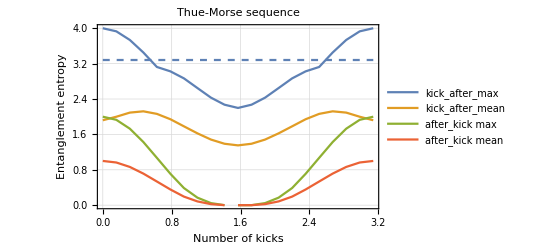

```mathematica
Show[ListLinePlot[{katcmmax,kactmmean,tmmax,tmmean},PlotTheme->"Detailed",PlotLegends->{"kick_after_max","kick_after_mean","after_kick max","after_kick mean","correct_max","correct_mean"}],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},PlotLabel->HoldForm[Thue-Morse sequence],LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotRange->All]
```

```mathematica
ListLinePlot[Drop[katmn[[1]],1]]
```

Part::partd: Part specification katmn⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: 1. is not a list of numbers or pairs of numbers.

ListLinePlot[1]

## dt = pi/32

#### data

```mathematica
tm32 = {-0.000000000000000000*10^+00,1.783237203716266261*10^+00,3.324858166046845476*10^+00,2.421153335052212530*10^+00,2.377685489294917076*10^+00,2.497402042346144491*10^+00,2.084525230059896650*10^+00,1.924849934983719590*10^+00,2.523686571384165411*10^+00,2.181075865234467948*10^+00,1.758889808869172011*10^+00,2.497921728281066844*10^+00,2.447578662875377731*10^+00,2.824736544977004993*10^+00,2.282756135383015028*10^+00,1.500665594476556786*10^+00,1.818586989639881857*10^+00,2.598509098625570335*10^+00,2.496069190105190572*10^+00,2.428587037810681082*10^+00,2.880187516914161527*10^+00,2.552373616425487768*10^+00,2.206128942987293229*10^+00,1.989512986712272280*10^+00,1.789673458636439562*10^+00,2.306428146912676169*10^+00,3.263197244215662263*10^+00,2.358523916769464268*10^+00,2.007283636434445295*10^+00,2.672116231651420648*10^+00,1.884739513681068068*10^+00,7.928767419577944509*10^-01,2.243876431999586529*10^+00,3.281942569726572057*10^+00,2.513461692430141614*10^+00,2.126794036368442775*10^+00,1.649243769891797218*10^+00,2.583803129956669942*10^+00,3.228597945827357485*10^+00,2.292902216239640190*10^+00,1.911826199098805468*10^+00,2.168398693634980390*10^+00,2.660679685707243003*10^+00,2.744397728195370867*10^+00,3.221821684788930273*10^+00,2.212285533638352675*10^+00,1.638532042276019229*10^+00,2.292841054249699084*10^+00,3.523682809979367558*10^+00,2.352652275060385989*10^+00,1.421637516122749689*10^+00,1.900727575112116874*10^+00,2.210123371164782302*10^+00,2.334168209369894331*10^+00,2.858672641669522285*10^+00,2.866427447555448538*10^+00,2.527873070431259528*10^+00,1.936077815753505016*10^+00,2.063778866407068868*10^+00,2.510041824802576649*10^+00,2.678110978589596236*10^+00,1.896588784334334976*10^+00,1.432717963322992283*10^+00,2.459499939677828095*10^+00,3.007783048382838942*10^+00,2.075622200487980962*10^+00,1.624656684061312806*10^+00,2.235338566079265732*10^+00,2.503230547928254168*10^+00,2.156904201305818614*10^+00,2.168083750720390057*10^+00,2.815355076746042684*10^+00,3.191380222049449156*10^+00,2.538763638866602612*10^+00,2.308658229161206332*10^+00,2.891698107378677829*10^+00,2.606391419974641632*10^+00,2.161688105679235417*10^+00,2.541947905821867693*10^+00,3.590981684978288957*10^+00,2.294382925689982589*10^+00,1.045553527735106680*10^+00,2.335046035775143469*10^+00,3.607080900329344253*10^+00,2.424359636405353680*10^+00,1.541638808203923627*10^+00,1.983900591680474168*10^+00,2.680195756957118647*10^+00,2.630165743682600255*10^+00,2.464661419082656124*10^+00,2.084450279375556381*10^+00,1.885221605361663055*10^+00,2.218275180716133388*10^+00,2.177496932368733873*10^+00,2.667859219983240493*10^+00,2.362527724241833660*10^+00,1.795875461735379597*10^+00,2.514223665769066862*10^+00,2.440389922392996347*10^+00,1.218512349017349727*10^+00,2.099348495911415924*10^+00,3.203341950341815014*10^+00,2.376521802233629632*10^+00,1.744288614220484979*10^+00,1.674041726584930334*10^+00,1.939646489636104310*10^+00,2.005510302636232201*10^+00,2.082410025294606726*10^+00,2.500187313443220205*10^+00,2.478724382772079959*10^+00,1.845559343875896374*10^+00,2.010067173343957680*10^+00,1.695426005350727960*10^+00,2.734227184241167397*10^+00,3.050550763947051269*10^+00,2.335228613819253063*10^+00,2.734582465338958102*10^+00,1.892327553838184517*10^+00,2.007551995279492019*10^+00,2.296851058267883161*10^+00,2.698084835216893129*10^+00,2.545177385592508834*10^+00,1.636861851677908541*10^+00,1.774569108942055440*10^+00,2.387668518732499745*10^+00,3.457214774447698424*10^+00,2.414192174867856977*10^+00,1.632514516667000537*10^+00,2.482603975087845694*10^+00,3.073218445345028194*10^+00,2.528709319900653618*10^+00,2.540059682869949320*10^+00,2.331936937935474852*10^+00,2.408473715485068833*10^+00,3.233876883302857941*10^+00,2.303162083356259160*10^+00,1.288809847202989856*10^+00,2.004175809231215410*10^+00,3.239114094081247952*10^+00,2.568650991301923536*10^+00,2.284682711344225847*10^+00,1.585109942749983070*10^+00,2.329305725826006146*10^+00,2.935239373980213173*10^+00,2.446453051646531929*10^+00,1.827829331006201041*10^+00,1.661725906861679425*10^+00,1.872018153089463954*10^+00,2.199647939311080158*10^+00,2.840109357543827873*10^+00,2.789798180046722642*10^+00,2.567123015270665221*10^+00,2.482887234659283848*10^+00,2.807467828860648495*10^+00,2.459161342118187044*10^+00,1.868566054957217171*10^+00,1.839675698207154486*10^+00,2.008662510018714542*10^+00,2.326235495141691256*10^+00,2.174426578123501486*10^+00,2.428468338405439741*10^+00,2.410298657547218504*10^+00,2.228086594987043423*10^+00,2.056990481506443036*10^+00,1.761005624547441695*10^+00,2.235329128962901368*10^+00,2.702514490441116912*10^+00,3.428518447455631168*10^+00,2.064877486423655206*10^+00,1.254895144647544925*10^+00,2.112362622586445138*10^+00,2.903021929570113624*10^+00,2.288086056739208285*10^+00,1.933377312653226987*10^+00,2.365207718754831490*10^+00,2.162985058600067401*10^+00,2.315029185348372209*10^+00,1.947825470746924914*10^+00,2.249566166580125426*10^+00,2.337907028777657992*10^+00,2.004915924183797049*10^+00,1.763312536528518049*10^+00,2.396955777188578551*10^+00,2.779524296816949569*10^+00,2.521562617230117098*10^+00,2.421819730230932333*10^+00,2.401733465121358435*10^+00,2.681905167269586165*10^+00,3.058146785040325444*10^+00,2.994452387776725732*10^+00,2.126291116871486864*10^+00,1.976259432523756132*10^+00,2.657134576936126980*10^+00,2.715339849433079156*10^+00,2.971736006927971907*10^+00,2.946876063292567238*10^+00,2.221315433458654898*10^+00,1.960454647409551221*10^+00,2.380040763576743768*10^+00,2.609796227875979202*10^+00,2.722912528242654327*10^-14,1.780820731443533589*10^+00,3.317197115270908103*10^+00,2.539944246305087194*10^+00,2.501331924644618177*10^+00,2.644555687634008834*10^+00,2.233261306851182404*10^+00,2.048214750625251046*10^+00,2.553921033121993922*10^+00,2.293290864505389770*10^+00,1.946571106284271435*10^+00,2.573587930371002308*10^+00,2.548521795179153671*10^+00,2.899266967365924152*10^+00,2.311713560827945990*10^+00,1.465605979782966362*10^+00,1.830083802041500451*10^+00,2.583259565771539812*10^+00,2.519988197290046195*10^+00,2.472103595401473175*10^+00,2.895241512394201688*10^+00,2.670656989349883936*10^+00,2.366055521654031324*10^+00,2.188168374985085318*10^+00,2.000860059887453080*10^+00,2.449431861962744428*10^+00,3.269171627734581698*10^+00,2.461419622926929840*10^+00,2.097050716146718674*10^+00,2.619713772961923315*10^+00,1.881078480171112677*10^+00,9.124744491321059581*10^-01,2.257652394345933455*10^+00,3.268462900222228296*10^+00,2.634980711126742925*10^+00,2.291786653604137580*10^+00,1.922285781887741019*10^+00,2.746141081511019433*10^+00,3.224731296327860708*10^+00,2.427671634905503861*10^+00,2.088089544226876093*10^+00,2.319327784977503804*10^+00,2.767471664660709152*10^+00,2.848204805316419286*10^+00,3.179388107489709903*10^+00,2.344931114178779197*10^+00,1.786936219546018112*10^+00,2.401612075455111572*10^+00,3.518778764462404229*10^+00,2.444783214490371837*10^+00,1.550298324137192818*10^+00,1.978572759087381616*10^+00,2.251525595360481358*10^+00,2.397871261725622816*10^+00,2.896976076305154635*10^+00,2.971483160988613648*10^+00,2.639944693488999850*10^+00,2.011122169292522077*10^+00,2.104583687412210580*10^+00,2.534608987144105985*10^+00,2.714018395479213641*10^+00,1.989826380932397498*10^+00,1.501231687861902309*10^+00,2.478637873981032858*10^+00,3.079710537485098598*10^+00,2.247444238055801513*10^+00,1.860849616736113710*10^+00,2.416207503759848052*10^+00,2.591658707632435554*10^+00,2.254256380643738122*10^+00,2.217529134965752657*10^+00,2.809100245205982560*10^+00,3.208566104006264297*10^+00,2.690567626358896902*10^+00,2.502467587275934324*10^+00,2.963608519427820553*10^+00,2.653413474308140785*10^+00,2.168305006866390272*10^+00,2.603913125380506788*10^+00,3.610657110896017485*10^+00,2.422171920706435611*10^+00,1.284706311928620615*10^+00,2.470432436119599728*10^+00,3.564373141826717717*10^+00,2.490312910878761166*10^+00,1.695253336844832592*10^+00,2.011354683865199000*10^+00,2.550020149158337635*10^+00,2.614481590515374876*10^+00,2.491621117529109863*10^+00,2.176300844406224400*10^+00,2.042845918227513824*10^+00,2.358936483517233285*10^+00,2.312208688651543831*10^+00,2.725447052059911002*10^+00,2.378233594243305937*10^+00,1.918259915597552379*10^+00,2.567308143143786747*10^+00,2.532504843066556433*10^+00,1.388288770867670330*10^+00,2.164952383960510041*10^+00,3.185360947391282505*10^+00,2.456672236153063515*10^+00,1.910939815564167699*10^+00,1.891561595889096337*10^+00,2.108543127028644992*10^+00,2.179244167181529690*10^+00,2.306602818495777640*10^+00,2.574528876419249102*10^+00,2.518470893122304322*10^+00,1.856165874130554894*10^+00,2.065209089914860296*10^+00,1.817499863690654083*10^+00,2.786031917340250352*10^+00,3.139870844700205499*10^+00,2.507534136546018644*10^+00,2.843123001729376487*10^+00,2.072921216079454787*10^+00,2.150629170740104623*10^+00,2.392882097849559297*10^+00,2.713637861464717194*10^+00,2.660248529811960694*10^+00,1.875200796034551587*10^+00,1.941667844998695713*10^+00,2.468108127057294432*10^+00,3.397691928537079686*10^+00,2.504537953228478830*10^+00,1.796345572654727940*10^+00,2.588720739729399867*10^+00,3.124188870196659806*10^+00,2.693390834702382719*10^+00,2.677996870931260709*10^+00,2.484636926922003664*10^+00,2.481945195782693681*10^+00,3.185121570976348515*10^+00,2.309869002665304372*10^+00,1.352244570156035941*10^+00,2.086721905002550503*10^+00,3.227784514718734066*10^+00,2.641093509037492293*10^+00,2.433071326290725089*10^+00,1.858245134068101434*10^+00,2.508839724672969673*10^+00,3.037742035158667697*10^+00,2.629666842950126870*10^+00,1.998034916226693491*10^+00,1.836294464474375054*10^+00,2.028623340657098151*10^+00,2.414818031532670606*10^+00,2.958057168513704926*10^+00,2.850464095088438121*10^+00,2.577129195261824712*10^+00,2.477505223397400425*10^+00,2.725035582679865342*10^+00,2.520507262787047509*10^+00,2.047548883211197435*10^+00,1.982594628203284470*10^+00,2.164375383601024438*10^+00,2.509703935570229305*10^+00,2.385009982186883537*10^+00,2.581362223679478429*10^+00,2.522299264369349814*10^+00,2.307204504111194154*10^+00,2.116499067517574773*10^+00,1.817204833014258503*10^+00,2.266135727324912086*10^+00,2.749205043934008774*10^+00,3.420688109527620036*10^+00,2.208548753470948700*10^+00,1.428510686994374890*10^+00,2.228949636908219123*10^+00,2.924315278860559530*10^+00,2.420149324493667375*10^+00,2.141167073126738263*10^+00,2.516930524186507423*10^+00,2.288997376840822717*10^+00,2.470365743848474072*10^+00,2.170571216292723538*10^+00,2.408692534707109534*10^+00,2.444552360264051316*10^+00,2.132306226379766301*10^+00,1.965746111824131948*10^+00,2.512848827577234267*10^+00,2.877425455131249254*10^+00,2.674938338154297490*10^+00,2.527116106084357661*10^+00,2.487828830488529874*10^+00,2.730448451310970803*10^+00,3.105471458161175313*10^+00,3.021044604758511998*10^+00,2.212724297714512733*10^+00,2.043394797451960176*10^+00,2.692948059458075249*10^+00,2.727004793006348571*10^+00,2.966189873458489057*10^+00,3.021193918147791813*10^+00,2.413526947909959475*10^+00,2.176498425720685415*10^+00,2.509431146903309262*10^+00,2.606670533135647005*10^+00,-9.610279511444755881*10^-16,1.773812292304951743*10^+00,3.295836343711325611*10^+00,2.738411411969920550*10^+00,2.732924148607743575*10^+00,2.872600534533855665*10^+00,2.450305179961272728*10^+00,2.203539996119025179*10^+00,2.563681720383896856*10^+00,2.460584024290493943*10^+00,2.276061395434163082*10^+00,2.666336606275189425*10^+00,2.733987912566618217*10^+00,3.077327620556262744*10^+00,2.355768252739171231*10^+00,1.406598491280786067*10^+00,1.862309269144097446*10^+00,2.554525769903785548*10^+00,2.604104941853639499*10^+00,2.580840332384031210*10^+00,2.936969417344002409*10^+00,2.898360859223193309*10^+00,2.627983795605318473*10^+00,2.494006734809843362*10^+00,2.385772333356839692*10^+00,2.699272876555442124*10^+00,3.292844483025553437*10^+00,2.636938092332727912*10^+00,2.259329670687892033*10^+00,2.508976839207158527*10^+00,1.901616200705854132*10^+00,1.158822350821088198*10^+00,2.291478084718858721*10^+00,3.198853516898021443*10^+00,2.804625418700294581*10^+00,2.585179623665588178*10^+00,2.388459696378435471*10^+00,2.968036127172545946*10^+00,3.182719505215575229*10^+00,2.693402955875379590*10^+00,2.427242456997169562*10^+00,2.559779741090647764*10^+00,2.939192027426460019*10^+00,3.005933163248464712*10^+00,3.097667969330912374*10^+00,2.569365360689213507*10^+00,2.066333373411093355*10^+00,2.614679488913413064*10^+00,3.485603113714028201*10^+00,2.576144193834213780*10^+00,1.819450785088497113*10^+00,2.152160728070315443*10^+00,2.304678215343143766*10^+00,2.495924707778689466*10^+00,2.952496209814850392*10^+00,3.162784496126316292*10^+00,2.832669983286707271*10^+00,2.110572891395458672*10^+00,2.136140765903350225*10^+00,2.544954845492040540*10^+00,2.790570885145317259*10^+00,2.192430468612590388*10^+00,1.670205784934086779*10^+00,2.542300288938930564*10^+00,3.243527168027587226*10^+00,2.557781817115497347*10^+00,2.266776640402859755*10^+00,2.654190011740809485*10^+00,2.717688956893537178*10^+00,2.458812042526437036*10^+00,2.349651399040820987*10^+00,2.780615198859126114*10^+00,3.198485117551476797*10^+00,2.880116384799383589*10^+00,2.803332010452385781*10^+00,3.151975487141022381*10^+00,2.725215001556113847*10^+00,2.152775327951668149*10^+00,2.694071953215015025*10^+00,3.580674308698165387*10^+00,2.571779200485029726*10^+00,1.659882063736029423*10^+00,2.727999086057560252*10^+00,3.429045210999786875*10^+00,2.596647598240744870*10^+00,1.981655866946223199*10^+00,2.059558409589409500*10^+00,2.265022330566617281*10^+00,2.566177368535408565*10^+00,2.556624163751499257*10^+00,2.332558074209479138*10^+00,2.285809329084672825*10^+00,2.617692011374360916*10^+00,2.606243451188013260*10^+00,2.839933559308269739*10^+00,2.448528803035170398*10^+00,2.127941756376181548*10^+00,2.676176844567032198*10^+00,2.708665570148487411*10^+00,1.741077456010516444*10^+00,2.253366188555077532*10^+00,3.100372212332893618*10^+00,2.560636643161489090*10^+00,2.197275464008840995*10^+00,2.223203700146049844*10^+00,2.345756830669158965*10^+00,2.454099953157087732*10^+00,2.637568141083913797*10^+00,2.758726583846604630*10^+00,2.572535991309953918*10^+00,1.857245577528104263*10^+00,2.188802303700775997*10^+00,2.115942846777264741*10^+00,2.902215566309591210*10^+00,3.289046571090715965*10^+00,2.789631759232048758*10^+00,2.980745637268835679*10^+00,2.335700882521450694*10^+00,2.418412602043852111*10^+00,2.567276729474031072*10^+00,2.747740609767166831*10^+00,2.847395154203634871*10^+00,2.290262661227874030*10^+00,2.169169356569679241*10^+00,2.566248024095155067*10^+00,3.265154165060987435*10^+00,2.735292287486418505*10^+00,2.165000444429031390*10^+00,2.773648700983394111*10^+00,3.175920294434424029*10^+00,2.893917580267031386*10^+00,2.951149150391238152*10^+00,2.759404798011267701*10^+00,2.605462446974530444*10^+00,3.039305921496283425*10^+00,2.330154621609213272*10^+00,1.503840098295343264*10^+00,2.261120116805194424*10^+00,3.202134510809488077*10^+00,2.734560413345522356*10^+00,2.697653898244142923*10^+00,2.326595748987669854*10^+00,2.789962666010703085*10^+00,3.157125456160905230*10^+00,2.820962866523625046*10^+00,2.282862644438941491*10^+00,2.120883259791114028*10^+00,2.294858690311767369*10^+00,2.725138172830263272*10^+00,3.162030865126603363*10^+00,3.000745863037034944*10^+00,2.612530203206934409*10^+00,2.444300785208747051*10^+00,2.565879077858127744*10^+00,2.628567843084812061*10^+00,2.461759844667807506*10^+00,2.231074142584433151*10^+00,2.342862634129179611*10^+00,2.799640369624684322*10^+00,2.698288192878974368*10^+00,2.785181961852653654*10^+00,2.659934647895506821*10^+00,2.412558087976353960*10^+00,2.166376089763351054*10^+00,1.961622221154892154*10^+00,2.359297350876016885*10^+00,2.793058541627413405*10^+00,3.374026049678426453*10^+00,2.480209705132437215*10^+00,1.816674128480470829*10^+00,2.419766157242049243*10^+00,2.937220360900546723*10^+00,2.597006948987153230*10^+00,2.452034712714510789*10^+00,2.707425663295929930*10^+00,2.490076905709987631*10^+00,2.671935004651122547*10^+00,2.485080186938077418*10^+00,2.667330012358555713*10^+00,2.587709327939331061*10^+00,2.302462841475399813*10^+00,2.295569161804790870*10^+00,2.697705208212033412*10^+00,3.012848146003678007*10^+00,2.941317194936039048*10^+00,2.750331172671395041*10^+00,2.632417897589601097*10^+00,2.852575443838400115*10^+00,3.187427952464325198*10^+00,3.041378248932852912*10^+00,2.317352037509631479*10^+00,2.127821120889674678*10^+00,2.714429438756112312*10^+00,2.741439889822515852*10^+00,2.954675865524837519*10^+00,3.150433415110520663*10^+00,2.666337749545459435*10^+00,2.470129858950369517*10^+00,2.678779710248495149*10^+00,2.561013372397391130*10^+00,9.610279511444749964*10^-16,1.762909576435359504*10^+00,3.264968393992131901*10^+00,2.871069026005933722*10^+00,2.883716627049182080*10^+00,3.028389440428270962*10^+00,2.559965170136376589*10^+00,2.136935138009490309*10^+00,2.371678900348049179*10^+00,2.527495585918273946*10^+00,2.544666519757931233*10^+00,2.735617685441722902*10^+00,2.887267132603509090*10^+00,3.231119885164212668*10^+00,2.416160861817309158*10^+00,1.379351839881190145*10^+00,1.920751332915622056*10^+00,2.548711081807025991*10^+00,2.674375074554586007*10^+00,2.701726195086552984*10^+00,3.004171722867873928*10^+00,3.085339102986035087*10^+00,2.824692679209339641*10^+00,2.763252120562471603*10^+00,2.702193481941051800*10^+00,2.909405407439982216*10^+00,3.313534073237473621*10^+00,2.782087034186876195*10^+00,2.388747261065136129*10^+00,2.426040230066769610*10^+00,1.925907655579516042*10^+00,1.458179337772672834*10^+00,2.324338275865196479*10^+00,3.069504701016537496*10^+00,2.906007052752745068*10^+00,2.770948432459737987*10^+00,2.749550840909007476*10^+00,3.034984987061069450*10^+00,3.083100459665697901*10^+00,2.937778525632649629*10^+00,2.710047871256433982*10^+00,2.738242456754092835*10^+00,3.095304552991004154*10^+00,3.094499461311134514*10^+00,3.003945586794730893*10^+00,2.744537723908964111*10^+00,2.362215219435975122*10^+00,2.793655012137186144*10^+00,3.406418609029677746*10^+00,2.661750579396882088*10^+00,2.141275450297775329*10^+00,2.340668347872790100*10^+00,2.355815548501644763*10^+00,2.569988697569429270*10^+00,2.978833121574375298*10^+00,3.299549192778091111*10^+00,2.956206612692661828*10^+00,2.105977194788123175*10^+00,2.083395682551449468*10^+00,2.505205649503812193*10^+00,2.864834287643821753*10^+00,2.338186847441710903*10^+00,1.823413392335583527*10^+00,2.615449739226348047*10^+00,3.336962750327288507*10^+00,2.789444805679583972*10^+00,2.558440367327503573*10^+00,2.776650141910653957*10^+00,2.777676387895090748*10^+00,2.653036444159419194*10^+00,2.486808196635785784*10^+00,2.739884777550078532*10^+00,3.064664063036615982*10^+00,2.951925465379855673*10^+00,2.978410938006356812*10^+00,3.326255529618544315*10^+00,2.777868455176505158*10^+00,2.080948492113420034*10^+00,2.727846520399705099*10^+00,3.419996619440097252*10^+00,2.601318793610854385*10^+00,2.007133112518239226*10^+00,2.935728803553126376*10^+00,3.198776978963048023*10^+00,2.617694645458458869*10^+00,2.239684876535758651*10^+00,2.105018914887983428*10^+00,2.033393555060064806*10^+00,2.533517367934178921*10^+00,2.618406961998023252*10^+00,2.453024057211566245*10^+00,2.493458190806179253*10^+00,2.860271751023065079*10^+00,2.840271083159768395*10^+00,2.894025686830100863*10^+00,2.547894495136929560*10^+00,2.350736016012507257*10^+00,2.780590348347254270*10^+00,2.841519139209539802*10^+00,2.067438006657207339*10^+00,2.298227232591812275*10^+00,2.933271878331844995*10^+00,2.637440265762222680*10^+00,2.500543286464377957*10^+00,2.478360222253416900*10^+00,2.462126009872168897*10^+00,2.629992679055987548*10^+00,2.823228513478876156*10^+00,2.905390492797190305*10^+00,2.572982727043915396*10^+00,1.849920494608532362*10^+00,2.335442057263767968*10^+00,2.467689438616624376*10^+00,3.034902548468842554*10^+00,3.362663916778112938*10^+00,2.956864914382366649*10^+00,3.018873570710984833*10^+00,2.485251988936088452*10^+00,2.592081411022471915*10^+00,2.686150260190947492*10^+00,2.759913459247576473*10^+00,2.972007839387311723*10^+00,2.617931501172116260*10^+00,2.276878214410835266*10^+00,2.625972469051327973*10^+00,3.186626995220538827*10^+00,2.956371532543518477*10^+00,2.524790948103234900*10^+00,2.922535542073118719*10^+00,3.114371216972732448*10^+00,2.964484332046566362*10^+00,3.167048764751395407*10^+00,2.986568064200269212*10^+00,2.654661501918546218*10^+00,2.814096607696825458*10^+00,2.340329809447366571*10^+00,1.665870120655525977*10^+00,2.435418878126511366*10^+00,3.193911896410327689*10^+00,2.782337129001787535*10^+00,2.870510627118736835*10^+00,2.731830072676472376*10^+00,3.004201486272270127*10^+00,3.133104229366767690*10^+00,2.833687497211479389*10^+00,2.462621390613835892*10^+00,2.321983160435243221*10^+00,2.498350726533382637*10^+00,2.927508939558775225*10^+00,3.258491903855047944*10^+00,3.092374070248858686*10^+00,2.644278318746850598*10^+00,2.373523278480274001*10^+00,2.376921489752181316*10^+00,2.703286085254593907*10^+00,2.825567925482822318*10^+00,2.434773827296360160*10^+00,2.423776798073629557*10^+00,3.004790872595675122*10^+00,2.925816372583722291*10^+00,2.852701378236731866*10^+00,2.657888505863990058*10^+00,2.414551627008341583*10^+00,2.096735040428483021*10^+00,2.048229290388740687*10^+00,2.459535499055084617*10^+00,2.814200798731503195*10^+00,3.261741337818223396*10^+00,2.721057450825954405*10^+00,2.160212894868938527*10^+00,2.551693534314781520*10^+00,2.880016137769880302*10^+00,2.672466672213452465*10^+00,2.657884153198653010*10^+00,2.788138085707982938*10^+00,2.618171587052468663*10^+00,2.747339076186732232*10^+00,2.676174980228114286*10^+00,2.827523448004485296*10^+00,2.682954504427367048*10^+00,2.418977892497442994*10^+00,2.551438013966722984*10^+00,2.822792346166460575*10^+00,3.083811166760618505*10^+00,3.165939337894227101*10^+00,2.928457339415741156*10^+00,2.739453101997058937*10^+00,2.993445053463033023*10^+00,3.244153002914518691*10^+00,3.038015111133849810*10^+00,2.360845927060410521*10^+00,2.132405110040947793*10^+00,2.668149322093970710*10^+00,2.745722753348872391*10^+00,2.973599434195818514*10^+00,3.209378386337840450*10^+00,2.800431055775866263*10^+00,2.629533924228708575*10^+00,2.738250406889718658*10^+00,2.483577679320474019*10^+00,4.805139755722374982*10^-16,1.749194328010245103*10^+00,3.229757238494286753*10^+00,2.904080285955406016*10^+00,2.914265297259827747*10^+00,3.102393871841443662*10^+00,2.530274490931439857*10^+00,1.850356293901689764*10^+00,2.001696632504294193*10^+00,2.458890897044614832*10^+00,2.676107898007685559*10^+00,2.773008516741381158*10^+00,2.990178017271168720*10^+00,3.292511590055882564*10^+00,2.483757216316516026*10^+00,1.452288504769523980*10^+00,1.999803266408418212*10^+00,2.549151496532134686*10^+00,2.702552118021376071*10^+00,2.812777257127680564*10^+00,3.106112710285527712*10^+00,3.181329586485013738*10^+00,2.952052762108329009*10^+00,2.920607083458023112*10^+00,2.864314559561650597*10^+00,3.037409178830537293*10^+00,3.316566142592646038*10^+00,2.840403460999171514*10^+00,2.495922078876373185*10^+00,2.448107745649720002*10^+00,1.994243147418990558*10^+00,1.746171266525699872*10^+00,2.438377114283267311*10^+00,2.972370340789888044*10^+00,2.935148941601642303*10^+00,2.846852860387058648*10^+00,2.877964951502902657*10^+00,2.934775158504090875*10^+00,2.961139025808826819*10^+00,3.135177571796803786*10^+00,2.854343617028968438*10^+00,2.799112667804108501*10^+00,3.241100983065094088*10^+00,3.091514411574022070*10^+00,2.897628980265767762*10^+00,2.845806978332872106*10^+00,2.637239238595018964*10^+00,2.924205496970372131*10^+00,3.336587732893317337*10^+00,2.790579605386566797*10^+00,2.535852213696136115*10^+00,2.487851178264794072*10^+00,2.397599921509673493*10^+00,2.605179832784447314*10^+00,3.006686582223754289*10^+00,3.359776602054441064*10^+00,2.962696187907027046*10^+00,2.019113888537414248*10^+00,1.987907690288315488*10^+00,2.497810261510887031*10^+00,2.840416694874502213*10^+00,2.348520846515927740*10^+00,1.872235180462571646*10^+00,2.647822611684539140*10^+00,3.335744045953712877*10^+00,2.956950673068104329*10^+00,2.747550685838294537*10^+00,2.879064177771922584*10^+00,2.864084684120095758*10^+00,2.812443195513883776*10^+00,2.590356306385694474*10^+00,2.661014514765427830*10^+00,2.792080859253172509*10^+00,2.923245511732262880*10^+00,3.039757691384569860*10^+00,3.397526030224227611*10^+00,2.837997509407790275*10^+00,2.170682840214559040*10^+00,2.766560327110435757*10^+00,3.194638463884793111*10^+00,2.570955990909295608*10^+00,2.301104530131179882*10^+00,2.986085106221963770*10^+00,2.947437029314848189*10^+00,2.566751444836385510*10^+00,2.434401577101088510*10^+00,2.226756098196238653*10^+00,1.970052530687102621*10^+00,2.500772314278318920*10^+00,2.622405177238673168*10^+00,2.500975425114912554*10^+00,2.684834708771473455*10^+00,3.048599275792257757*10^+00,2.937847090320484966*10^+00,2.898114787323362584*10^+00,2.696480299977288553*10^+00,2.551492000048154019*10^+00,2.899035946772383188*10^+00,2.896671776875661131*10^+00,2.267942134301447865*10^+00,2.296553375675527864*10^+00,2.761054806453349109*10^+00,2.730742338430633520*10^+00,2.750089606236347795*10^+00,2.637268463922465944*10^+00,2.525388098148128702*10^+00,2.662503998452863119*10^+00,2.835296189990283988*10^+00,2.928283087780009009*10^+00,2.472163412095623070*10^+00,1.831207789037234246*10^+00,2.489801861823297990*10^+00,2.765880536624727437*10^+00,3.121290087060929253*10^+00,3.309292018448294126*10^+00,2.996251739327347785*10^+00,2.931791419446502900*10^+00,2.498815230113689445*10^+00,2.612448996324452821*10^+00,2.710243586466177135*10^+00,2.749461830058377299*10^+00,3.021189701183779608*10^+00,2.777059961683563394*10^+00,2.319025283246812119*10^+00,2.675088924855287154*10^+00,3.171089857165490855*10^+00,3.102893953535197813*10^+00,2.789252302106683512*10^+00,3.007701020290225014*10^+00,3.010168902329536600*10^+00,2.899451461735136348*10^+00,3.252184944778051090*10^+00,3.101860292416066311*10^+00,2.638803053428946388*10^+00,2.579122055429807325*10^+00,2.315938695419277327*10^+00,1.843013134248332907*10^+00,2.614295202260759066*10^+00,3.244824802425290144*10^+00,2.787537246998150753*10^+00,2.850811924238056072*10^+00,2.958645379266731990*10^+00,3.104988827359062675*10^+00,2.987549664402211924*10^+00,2.688949433205892969*10^+00,2.500514575677635243*10^+00,2.430708485463276780*10^+00,2.622025199122973049*10^+00,2.990539622224908545*10^+00,3.225771230306051507*10^+00,3.122926651312655011*10^+00,2.705951830825061855*10^+00,2.386288379745568733*10^+00,2.336053250274507054*10^+00,2.772683960226609123*10^+00,3.003673433372777701*10^+00,2.617989190868912797*10^+00,2.496804288433445596*10^+00,3.065458669335690889*10^+00,3.030859100981236232*10^+00,2.772437613722229521*10^+00,2.532022974524034353*10^+00,2.323516407589239385*10^+00,1.953512469269347074*10^+00,2.062458202811023433*10^+00,2.543553612632440064*10^+00,2.793530458209194212*10^+00,3.112275443647380513*10^+00,2.862649300108470740*10^+00,2.420403780512922154*10^+00,2.619845966569752882*10^+00,2.768714847699938364*10^+00,2.643930004099607434*10^+00,2.725125350881405506*10^+00,2.769884162001750028*10^+00,2.730767779260291128*10^+00,2.722114728792409011*10^+00,2.694244757538007740*10^+00,2.866529365416812691*10^+00,2.761863833370537868*10^+00,2.515033596727303422*10^+00,2.733600700910736592*10^+00,2.878430155478760355*10^+00,3.131643580062949184*10^+00,3.294778893295361222*10^+00,2.996012352664470857*10^+00,2.792737968292077433*10^+00,3.139102605015358982*10^+00,3.269924283869774406*10^+00,3.019353827204152907*10^+00,2.356227749341739397*10^+00,2.098900380969608293*10^+00,2.564828066742803170*10^+00,2.765420770284478635*10^+00,3.042817398214777924*10^+00,3.205605586774268989*10^+00,2.786297837789200926*10^+00,2.636175558331966151*10^+00,2.714867053494139704*10^+00,2.438629760298812954*10^+00,3.203426503814917641*10^-16,1.734020978688510795*10^+00,3.194779953313931831*10^+00,2.852104344681077652*10^+00,2.878457187453249411*10^+00,3.139240868149964392*10^+00,2.456567265979463510*10^+00,1.494170350545618975*10^+00,1.605156132247600675*10^+00,2.318039896253465404*10^+00,2.686827527234276314*10^+00,2.798098055483277058*10^+00,3.089195522514720960*10^+00,3.277701456063273344*10^+00,2.553115213405410255*10^+00,1.640656964418064190*10^+00,2.139298113980331983*10^+00,2.546060551130387317*10^+00,2.718530346045370027*10^+00,2.908043618571491518*10^+00,3.209084905316353709*10^+00,3.201708606279930258*10^+00,3.026338038324188240*10^+00,3.016098973735251931*10^+00,2.902759337546590324*10^+00,3.080871187403566136*10^+00,3.284606932776772847*10^+00,2.831860742005139375*10^+00,2.612940548222471016*10^+00,2.553285180026106271*10^+00,2.099350036893386395*10^+00,1.989741166236566272*10^+00,2.652734605209178476*10^+00,2.975596285025533305*10^+00,2.942667153789515488*10^+00,2.878703024704233115*10^+00,2.854173277727279689*10^+00,2.749153285289712478*10^+00,2.883921827258178361*10^+00,3.225222512708762590*10^+00,2.865270221053679567*10^+00,2.759252879123991864*10^+00,3.326546927867207515*10^+00,3.033682729989227056*10^+00,2.799022361651838597*10^+00,2.920734554952565176*10^+00,2.829000303526479243*10^+00,2.985260681746647826*10^+00,3.323310229951636607*10^+00,2.943338643698581780*10^+00,2.895035055487073183*10^+00,2.546574069398445772*10^+00,2.452723371801363683*10^+00,2.619733413909978381*10^+00,3.047893370054865159*10^+00,3.361617840301700078*10^+00,2.905405310567571231*10^+00,1.908030883776420161*10^+00,1.900197912530548816*10^+00,2.461228840910136828*10^+00,2.716626167007368142*10^+00,2.240920945182509172*10^+00,1.826413072868086518*10^+00,2.667613999328249719*10^+00,3.352872581080636571*10^+00,3.080942721777451432*10^+00,2.879448874732118302*10^+00,3.047634123154209451*10^+00,3.010004922495555402*10^+00,2.962112251080634806*10^+00,2.664501832528328507*10^+00,2.533013786029571168*10^+00,2.461158636710881531*10^+00,2.840384190307744916*10^+00,3.014651047721375487*10^+00,3.363532293815096441*10^+00,2.965136198002175316*10^+00,2.477614760515236103*10^+00,2.905345254090933249*10^+00,3.027255906913564942*10^+00,2.547239250275782574*10^+00,2.556841080645081199*10^+00,2.904447920435452968*10^+00,2.735102689622199712*10^+00,2.514572706457578910*10^+00,2.557990478650381760*10^+00,2.393607312754640670*10^+00,2.138588910291441714*10^+00,2.544523165012093191*10^+00,2.568429504480009840*10^+00,2.460253664413007524*10^+00,2.834494437002656575*10^+00,3.178109399836243298*10^+00,2.919195560759300534*10^+00,2.860016672002706706*10^+00,2.838478972529492328*10^+00,2.746581415782165081*10^+00,3.062202679310491060*10^+00,2.906653735392285220*10^+00,2.298214058819091576*10^+00,2.263559359352594669*10^+00,2.675635873122991004*10^+00,2.864990230296768914*10^+00,2.970479594268948809*10^+00,2.748872696818768446*10^+00,2.577354537764052544*10^+00,2.630189103116790772*10^+00,2.700234804414808565*10^+00,2.811409840628905865*10^+00,2.290520386582083123*10^+00,1.827345624595595464*10^+00,2.633323702342376116*10^+00,2.984680720370785245*10^+00,3.140784939269504861*10^+00,3.167582536777542757*10^+00,2.954281106733571249*10^+00,2.823650125901996155*10^+00,2.492327941160416227*10^+00,2.523181314798493169*10^+00,2.669833690644440871*10^+00,2.773275587662926700*10^+00,3.050705194586673663*10^+00,2.816790218495350384*10^+00,2.362981451910865616*10^+00,2.757948576339325442*10^+00,3.186216918671313181*10^+00,3.111185573830729911*10^+00,2.876509083982961457*10^+00,3.050139202333216115*10^+00,2.939312939482594533*10^+00,2.825241410424624178*10^+00,3.254436407418715760*10^+00,3.129155293797377002*10^+00,2.636826056246188710*10^+00,2.380824641280748999*10^+00,2.290294927056978125*10^+00,2.049935277676768752*10^+00,2.782377066545687949*10^+00,3.339242611348166356*10^+00,2.784664723824074706*10^+00,2.709504248954290428*10^+00,3.018198214370050092*10^+00,3.146784755835758673*10^+00,2.864655381095324582*10^+00,2.499510354320837457*10^+00,2.461888365548042579*10^+00,2.463283082789865741*10^+00,2.680029000663373573*10^+00,2.972565106089013920*10^+00,3.134958400371496090*10^+00,3.117006517960143608*10^+00,2.798386755668200720*10^+00,2.582039784931403847*10^+00,2.539581033856300074*10^+00,2.871784052583558733*10^+00,2.975409110924807532*10^+00,2.738578739149556185*10^+00,2.657338839687319876*10^+00,3.048689934617649921*10^+00,3.064459533269718428*10^+00,2.640280593436942436*10^+00,2.424591863979891126*10^+00,2.227140783872805230*10^+00,1.859385401122545911*10^+00,2.053646696713995468*10^+00,2.585402724282821474*10^+00,2.752839902305998621*10^+00,2.977516290377987485*10^+00,2.951174063847133766*10^+00,2.607111928376261378*10^+00,2.667523157912107035*10^+00,2.735382996494509111*10^+00,2.616774100348198573*10^+00,2.754728379134543825*10^+00,2.775468268293957319*10^+00,2.903579556472802192*10^+00,2.743827428002582280*10^+00,2.628921509477856855*10^+00,2.874856531955662486*10^+00,2.831773597404019682*10^+00,2.559728039640702058*10^+00,2.796806550798001112*10^+00,2.900991306324075314*10^+00,3.188373593830019281*10^+00,3.345292046563471899*10^+00,2.943499341378866152*10^+00,2.834321811083167386*10^+00,3.289857605640437388*10^+00,3.271809387749517573*10^+00,3.015531485492322972*10^+00,2.386121917367391099*10^+00,2.062343388633100183*10^+00,2.445732132417196780*10^+00,2.746622602047326112*10^+00,3.147693329952002905*10^+00,3.143115658109642219*10^+00,2.724665871961214236*10^+00,2.627153833166262942*10^+00,2.694519097980093036*10^+00,2.453365283361276461*10^+00,-9.610279511444755881*10^-16,1.718879513406899262*10^+00,3.163312015375296937*10^+00,2.812066796933765822*10^+00,2.845396340455334183*10^+00,3.198044526888884853*10^+00,2.400312132700718415*10^+00,1.221173123135057548*10^+00,1.357392675198499488*10^+00,2.229104415055492616*10^+00,2.638584208786157959*10^+00,2.851579984041443083*10^+00,3.181936105804295423*10^+00,3.224276047501218212*10^+00,2.569235079404688538*10^+00,1.870185908764225857*10^+00,2.282986575438262999*10^+00,2.582491015776625431*10^+00,2.724165214163602577*10^+00,2.997352541663063086*10^+00,3.282277275307223796*10^+00,3.203264046516638430*10^+00,3.062493699592351959*10^+00,3.074336739924341977*10^+00,2.858614162627979738*10^+00,3.027200179135138391*10^+00,3.190930057909005413*10^+00,2.802313238286226582*10^+00,2.722341929984908759*10^+00,2.701637329246621810*10^+00,2.228707655497359941*10^+00,2.182757991972538392*10^+00,2.882455240916982575*10^+00,3.032959886549142059*10^+00,2.991971074837040501*10^+00,2.981071710198469837*10^+00,2.846006157489762600*10^+00,2.615076108372882846*10^+00,2.867943442695041867*10^+00,3.229590624307296487*10^+00,2.792776626340432777*10^+00,2.703105648606373812*10^+00,3.312896875302372202*10^+00,2.965386635653898928*10^+00,2.730344977665871475*10^+00,2.978813875449502380*10^+00,2.917446753033804185*10^+00,3.010112966473363016*10^+00,3.336324746951577325*10^+00,3.121378737614993515*10^+00,3.133294569781466254*10^+00,2.525007530075885853*10^+00,2.494987214737357739*10^+00,2.689412530822744785*10^+00,3.093095922107058193*10^+00,3.298851604667535575*10^+00,2.834445028744066342*10^+00,1.841361239555700635*10^+00,1.808457021390217578*10^+00,2.382171092105339838*10^+00,2.566265382230224823*10^+00,2.098018672454095679*10^+00,1.758874909238211215*10^+00,2.667177843555003314*10^+00,3.435325967859972796*10^+00,3.168423886920229915*10^+00,3.017740790238177429*10^+00,3.257976010758449004*10^+00,3.147100127895377852*10^+00,3.078146341621915028*10^+00,2.704121537413883836*10^+00,2.400464922973766235*10^+00,2.281380184660690702*10^+00,2.763307298064748174*10^+00,2.929629707555976736*10^+00,3.262550877622752310*10^+00,3.079151789457787558*10^+00,2.840977841797797332*10^+00,3.087596318975641019*10^+00,2.960675478060398547*10^+00,2.534716766184910153*10^+00,2.743836754177841009*10^+00,2.812980174296881408*10^+00,2.623956465247318626*10^+00,2.525585028944115074*10^+00,2.663360575677764075*10^+00,2.584328336195044873*10^+00,2.425950000617048907*10^+00,2.615209814465844218*10^+00,2.450985856524587891*10^+00,2.331669213967590526*10^+00,2.862280907045710698*10^+00,3.214084382361873438*10^+00,2.833440552796469003*10^+00,2.806544518215475126*10^+00,2.941243622186435314*10^+00,2.888624121276895274*10^+00,3.206664221341353649*10^+00,2.890950811055926106*10^+00,2.211501682440873751*10^+00,2.170443290630962974*10^+00,2.681889306104391579*10^+00,3.068079960550932572*10^+00,3.151061632581589222*10^+00,2.829735825367858837*10^+00,2.570517555311160773*10^+00,2.527695766357716867*10^+00,2.527060951338085726*10^+00,2.591695566009059704*10^+00,2.062018750194175354*10^+00,1.802221860933118647*10^+00,2.733864817293763849*10^+00,3.102352974389676721*10^+00,3.104585534851537432*10^+00,2.988494555236676398*10^+00,2.895445653128006835*10^+00,2.811818998208565734*10^+00,2.540903409829959436*10^+00,2.449449039850891019*10^+00,2.612413119722658550*10^+00,2.878838704427042039*10^+00,3.094172215615011101*10^+00,2.829852838532543213*10^+00,2.424298396594828819*10^+00,2.828439465547845089*10^+00,3.209649155745742277*10^+00,3.001569048327548117*10^+00,2.831108149028604970*10^+00,3.052799088781915415*10^+00,2.970430292767475056*10^+00,2.833112954008327744*10^+00,3.223344420599058679*10^+00,3.077997162695101707*10^+00,2.667683331414457015*10^+00,2.397413538231897956*10^+00,2.311717285728474014*10^+00,2.251229946299101226*10^+00,2.947060163971543467*10^+00,3.423978232660535692*10^+00,2.802606483387543257*10^+00,2.566609948651199957*10^+00,2.996626754213375321*10^+00,3.179225194783159125*10^+00,2.838498428246622574*10^+00,2.429270858147988488*10^+00,2.417526342927429184*10^+00,2.471996279415908049*10^+00,2.678794935780870468*10^+00,2.944756734526953412*10^+00,3.041849545009535305*10^+00,3.090160065099624376*10^+00,2.920342507158911971*10^+00,2.770873649185239707*10^+00,2.831262754059110875*10^+00,2.949506298151737038*10^+00,2.801218249354270107*10^+00,2.740325113928320455*10^+00,2.843080174387287329*10^+00,3.019918074652513607*10^+00,3.076046701427925356*10^+00,2.579842621891324406*10^+00,2.387738209809707968*10^+00,2.223605196272282924*10^+00,1.871380386421487962*10^+00,2.044267431118864664*10^+00,2.540910472806994669*10^+00,2.632010030148070889*10^+00,2.899634791344683382*10^+00,3.086154031018796484*10^+00,2.746444506809106123*10^+00,2.719630946045453523*10^+00,2.772412542369809163*10^+00,2.604960286726799357*10^+00,2.768044771715731045*10^+00,2.835032108467127276*10^+00,3.097550683883667499*10^+00,2.829753132818705996*10^+00,2.568190057522675929*10^+00,2.852340549235072409*10^+00,2.850678837757997020*10^+00,2.573261063911466806*10^+00,2.776275969551606604*10^+00,2.897685643994456495*10^+00,3.242783765084374270*10^+00,3.328575290920595453*10^+00,2.817127857472565111*10^+00,2.887739636358034989*10^+00,3.406463963665774308*10^+00,3.278209604031392832*10^+00,3.029436292291204147*10^+00,2.449206992539274985*10^+00,2.102169564626496179*10^+00,2.310615385076791206*10^+00,2.734142993572739044*10^+00,3.221966370748299724*10^+00,3.071225606912578066*10^+00,2.654770271030880036*10^+00,2.635979416936228059*10^+00,2.714672404790507088*10^+00,2.529013947582960942*10^+00,-3.203426503814917641*10^-16,1.705247740374219445*10^+00,3.137551922650418490*10^+00,2.785588393244831984*10^+00,2.839558860813741870*10^+00,3.281899600500823411*10^+00,2.365485045083218996*10^+00,1.145001367503799106*10^+00,1.280626665012908560*10^+00,2.235540482235356397*10^+00,2.582212342958490225*10^+00,2.904434094311512560*10^+00,3.254464696887502839*10^+00,3.175794739955946078*10^+00,2.559833577407516714*10^+00,2.058769583352804133*10^+00,2.395192591169725382*10^+00,2.631539266016678091*10^+00,2.733244269260085790*10^+00,3.077441941741819065*10^+00,3.320945092811247612*10^+00,3.181896713577760050*10^+00,3.097750169449624114*10^+00,3.125620501733185286*10^+00,2.770266242621781672*10^+00,2.909361973122861933*10^+00,3.092882058919293797*10^+00,2.764929576336702333*10^+00,2.814225200379477876*10^+00,2.819900724706780437*10^+00,2.308257630081455680*10^+00,2.318890870113693659*10^+00,3.061559573178410432*10^+00,3.090293247819658085*10^+00,3.064634780054532825*10^+00,3.129322762121559798*10^+00,2.963007577499119805*10^+00,2.575453734767838121*10^+00,2.894738868307383139*10^+00,3.211786931853152005*10^+00,2.700718383853704108*10^+00,2.668953339806038549*10^+00,3.237996003721215210*10^+00,2.912483560003299665*10^+00,2.701773796785309489*10^+00,3.007576945149356362*10^+00,2.930977276207215265*10^+00,3.025521995313186885*10^+00,3.361410365110248044*10^+00,3.248221915358889600*10^+00,3.223188648894645514*10^+00,2.457420611664308918*10^+00,2.510853547435041300*10^+00,2.752103918378682401*10^+00,3.067089156747980105*10^+00,3.210551030338378631*10^+00,2.780373268340003978*10^+00,1.796398691787201463*10^+00,1.727062168856285496*10^+00,2.297985508889220707*10^+00,2.471254740828189078*10^+00,2.034830384434275441*10^+00,1.743186548778447253*10^+00,2.667530497001548984*10^+00,3.489496824197806824*10^+00,3.203629640323976790*10^+00,3.128155884848305757*10^+00,3.443259339829024768*10^+00,3.269653317953423510*10^+00,3.141282046622037250*10^+00,2.742963365322093061*10^+00,2.337364195489014751*10^+00,2.286931858594823286*10^+00,2.751485134900351959*10^+00,2.844734028325019537*10^+00,3.131458385188242488*10^+00,3.093563636832458386*10^+00,3.107607472541990656*10^+00,3.251065894282268331*10^+00,2.938189174573311302*10^+00,2.516381396516515156*10^+00,2.880445865784452941*10^+00,2.766294980331553077*10^+00,2.598151381414509409*10^+00,2.560790203821321498*10^+00,2.754267782018695598*10^+00,2.748212228987606753*10^+00,2.679595150895044853*10^+00,2.658503737278909984*10^+00,2.317523136568914843*10^+00,2.168660901896936721*10^+00,2.778567565359753466*10^+00,3.149318563744984978*10^+00,2.754866496022255973*10^+00,2.768998303317518506*10^+00,2.963915382723699032*10^+00,2.954190294685667517*10^+00,3.305770875624906679*10^+00,2.882909264584954556*10^+00,2.060587335486416816*10^+00,2.067377406631373482*10^+00,2.719230194883542229*10^+00,3.262478320637044682*10^+00,3.273231739770383175*10^+00,2.910195063554223083*10^+00,2.516344797025463542*10^+00,2.393292465319892148*10^+00,2.418305259077770941*10^+00,2.393896705350762044*10^+00,1.871302184083519560*10^+00,1.775076767175313375*10^+00,2.797159897704307951*10^+00,3.176354849671263469*10^+00,3.039796021453423425*10^+00,2.825004510376861955*10^+00,2.842070995312887316*10^+00,2.867997340156176023*10^+00,2.632020618095976872*10^+00,2.394090627752613720*10^+00,2.604579134330281320*10^+00,3.066043612980262623*10^+00,3.136414404960182534*10^+00,2.871183464205179003*10^+00,2.517040265620942741*10^+00,2.856722133307351363*10^+00,3.179434955418992459*10^+00,2.828243896125341550*10^+00,2.717500506070804178*10^+00,3.048024520737011134*10^+00,3.047224566705011295*10^+00,2.889561351477011542*10^+00,3.186519878894395141*10^+00,3.008502514793233384*10^+00,2.740793284609602587*10^+00,2.540247717540180084*10^+00,2.438598934036008359*10^+00,2.427274920912575240*10^+00,3.081980690014710866*10^+00,3.483900951746170094*10^+00,2.826340873114504770*10^+00,2.505152454429295794*10^+00,2.959486856910579000*10^+00,3.230422012761365202*10^+00,2.883798826070577803*10^+00,2.455475098037386061*10^+00,2.414415791795064159*10^+00,2.465229657418330778*10^+00,2.655022633756357386*10^+00,2.946174882182488908*10^+00,2.952136319474679471*10^+00,3.039747018296962811*10^+00,2.991342148505319543*10^+00,2.894843712213813536*10^+00,3.029467792241022916*10^+00,2.971317037572601016*10^+00,2.571064321031554911*10^+00,2.637240413711907649*10^+00,2.989827852718963896*10^+00,3.015968066214531618*10^+00,3.087838648140312614*10^+00,2.629668067194965264*10^+00,2.424599889986011725*10^+00,2.330347763321414689*10^+00,1.976523268240945708*10^+00,2.009952628042328548*10^+00,2.395058186893296082*10^+00,2.475202815885424013*10^+00,2.875513745010189304*10^+00,3.201565741046478841*10^+00,2.839128259017539513*10^+00,2.734499054098897819*10^+00,2.795099830337414826*10^+00,2.635847033153530639*10^+00,2.803619492843259398*10^+00,2.935853138820030406*10^+00,3.230520764595856686*10^+00,2.866787636399952710*10^+00,2.500835048645890790*10^+00,2.802088578127716278*10^+00,2.827511455323418854*10^+00,2.543114231071736953*10^+00,2.728080964550043674*10^+00,2.858904398678100645*10^+00,3.255370303386929454*10^+00,3.264517542900463809*10^+00,2.693191666852847721*10^+00,2.903107742665529845*10^+00,3.483178968616071458*10^+00,3.326210060183370398*10^+00,3.067520266756616376*10^+00,2.540583183357431718*10^+00,2.157368947850402563*10^+00,2.217213308188503706*10^+00,2.695731892715611533*10^+00,3.226098692335242824*10^+00,3.009966754377307652*10^+00,2.641239287242717726*10^+00,2.625905345043979544*10^+00,2.745150407262487935*10^+00,2.617285860328193881*10^+00,-3.203426503814917641*10^-16,1.694448209547768647*10^+00,3.119217887442611747*10^+00,2.768899490182589851*10^+00,2.835604854770537919*10^+00,3.345521068637227202*10^+00,2.392857879039621771*10^+00,1.227178044530162104*10^+00,1.359120964336283599*10^+00,2.289335189286590300*10^+00,2.594778427601982074*10^+00,2.953050254758056603*10^+00,3.253432697579881960*10^+00,3.110214611537743590*10^+00,2.537003536899946177*10^+00,2.176795367195979214*10^+00,2.469216080261992907*10^+00,2.677414577675450325*10^+00,2.755750181042309954*10^+00,3.114951125749474414*10^+00,3.320740000318877616*10^+00,3.135783576436210751*10^+00,3.106492357525456605*10^+00,3.136194532141626468*10^+00,2.669877629386336437*10^+00,2.749514960265160290*10^+00,3.004180659633572059*10^+00,2.699148688624739556*10^+00,2.843095821791457922*10^+00,2.838442051354684192*10^+00,2.336908764386785187*10^+00,2.404640435693217615*10^+00,3.184043078748450384*10^+00,3.124104679632226045*10^+00,3.094945284349249093*10^+00,3.245169043407859721*10^+00,3.086574139213316137*10^+00,2.575429556926073893*10^+00,2.942007588696188503*10^+00,3.188864756710149795*10^+00,2.667160995948055557*10^+00,2.665815862173986694*10^+00,3.173481959953803777*10^+00,2.885227512786056714*10^+00,2.707942467306299061*10^+00,3.001971587742646275*10^+00,2.896641576418045538*10^+00,3.050617294628511722*10^+00,3.375743609518261579*10^+00,3.296121439701320543*10^+00,3.200026315550854594*10^+00,2.461088946039073022*10^+00,2.518031735624728817*10^+00,2.784639530105176952*10^+00,2.966786642783564520*10^+00,3.114178925454015534*10^+00,2.756683789026369791*10^+00,1.805380424519330118*10^+00,1.711851210006603230*10^+00,2.268214708764639820*10^+00,2.504108669311180257*10^+00,2.067741940470928963*10^+00,1.819408509414908615*10^+00,2.682052391728551033*10^+00,3.458245181589815420*10^+00,3.172300981232119899*10^+00,3.161788869379233979*10^+00,3.539775498841096102*10^+00,3.355887316058645542*10^+00,3.145519524722141469*10^+00,2.784412732380842304*10^+00,2.383237315687609659*10^+00,2.460688682420904883*10^+00,2.804194118882692432*10^+00,2.798791604306357428*10^+00,2.989498448873344927*10^+00,3.081577700875167913*10^+00,3.235407992112087960*10^+00,3.329524577462466439*10^+00,2.899262566518298723*10^+00,2.445678596796650783*10^+00,2.949932126477534666*10^+00,2.788390688275661500*10^+00,2.602705306755443093*10^+00,2.618879110267507304*10^+00,2.796709616563350487*10^+00,2.851919074545899768*10^+00,2.834795445253186941*10^+00,2.606693471932275852*10^+00,2.190631771640737302*10^+00,2.045316388135055785*10^+00,2.630769576586621472*10^+00,3.003123122261855293*10^+00,2.703913136527653194*10^+00,2.755674401620723302*10^+00,2.926516827608599325*10^+00,2.945536438671271906*10^+00,3.315425026609069903*10^+00,2.859530196310732908*10^+00,1.951204002246121227*10^+00,2.004269231324053990*10^+00,2.748179603820057437*10^+00,3.343730101733945581*10^+00,3.299285870182802505*10^+00,2.951363864178500496*10^+00,2.477818339860908381*10^+00,2.339332945884990078*10^+00,2.447337500903609353*10^+00,2.294133418994655393*10^+00,1.757128235615899037*10^+00,1.763065855396578785*10^+00,2.821331525881652702*10^+00,3.217956021588912918*10^+00,2.974137531036129989*10^+00,2.711799943116033340*10^+00,2.859297560243725833*10^+00,2.939973707689429006*10^+00,2.740642070811034614*10^+00,2.352862610498323903*10^+00,2.622410955111627029*10^+00,3.235664360290724684*10^+00,3.197424502319832218*10^+00,2.918412963463635101*10^+00,2.622189899095301868*10^+00,2.885167279134780216*10^+00,3.106147475279917636*10^+00,2.646811332894998259*10^+00,2.595745723389465631*10^+00,3.049451534917082540*10^+00,3.139402626530861440*10^+00,2.942349037591160954*10^+00,3.150661711703912182*10^+00,2.966079635582239415*10^+00,2.844744613034049685*10^+00,2.668838822944660016*10^+00,2.553683975802001349*10^+00,2.517108695430986920*10^+00,3.140009059093098021*10^+00,3.516397127874219652*10^+00,2.865053547665557865*10^+00,2.548824015099501850*10^+00,2.957767808036892099*10^+00,3.305043462554656308*10^+00,2.949106838695364274*10^+00,2.521026369801684375*10^+00,2.439482373220484668*10^+00,2.496948433815311841*10^+00,2.665251722324605499*10^+00,2.940661591895797233*10^+00,2.886360964093068304*10^+00,3.018287726543165128*10^+00,3.067268479410191429*10^+00,2.954745628828533199*10^+00,3.066141336010548279*10^+00,2.905898583979254823*10^+00,2.392952942678782335*10^+00,2.475024097620123431*10^+00,3.067906519039884206*10^+00,3.032681524697252939*10^+00,3.092258419258114177*10^+00,2.721050936436126833*10^+00,2.577758882952620567*10^+00,2.449425034417785696*10^+00,2.081674310070069200*10^+00,1.935849426485431568*10^+00,2.187634073330440909*10^+00,2.342719821515461209*10^+00,2.840765090495819489*10^+00,3.249465080634811542*10^+00,2.873592293485888405*10^+00,2.736015520195554274*10^+00,2.781995176079321119*10^+00,2.653986459290034627*10^+00,2.826636398922538262*10^+00,2.990084577169277669*10^+00,3.239858143190972317*10^+00,2.835247165572775341*10^+00,2.480767477160446433*10^+00,2.748827349961969979*10^+00,2.795027196108804013*10^+00,2.531201474202860791*10^+00,2.683031500114667622*10^+00,2.807438125546427798*10^+00,3.186311691989188066*10^+00,3.181726733884259861*10^+00,2.676139559577213500*10^+00,2.919956510093555835*10^+00,3.506985186049821124*10^+00,3.382352496916127826*10^+00,3.110001540524784502*10^+00,2.642703245530941381*10^+00,2.229687797235456514*10^+00,2.227273414123702278*10^+00,2.681625719934602969*10^+00,3.158041103924640325*10^+00,2.983206181710129190*10^+00,2.637020424473528912*10^+00,2.582067869611528899*10^+00,2.761036022504116616*10^+00,2.694391526452551755*10^+00,-9.610279511444755881*10^-16,1.687523251923939149*10^+00,3.109841393726922476*10^+00,2.742652578527340346*10^+00,2.808507474556851680*10^+00,3.357684358062143826*10^+00,2.477015729387293863*10^+00,1.444244706954619373*10^+00,1.523511075950756855*10^+00,2.359255381358752235*10^+00,2.654277059518886261*10^+00,2.985352142830135502*10^+00,3.170557001954082299*10^+00,3.025759765891935515*10^+00,2.487358196645701014*10^+00,2.198424604378817371*10^+00,2.471015415649246094*10^+00,2.679967592829166634*10^+00,2.756487243183929792*10^+00,3.078547096256274429*10^+00,3.235954786164358499*10^+00,3.042306393934149256*10^+00,3.090968370149250521*10^+00,3.091424804556507588*10^+00,2.614503090759973780*10^+00,2.615946608297052389*10^+00,2.965894396419821444*10^+00,2.611388000154347022*10^+00,2.778422514948987398*10^+00,2.754126861047294206*10^+00,2.315272913334817328*10^+00,2.452875292288182685*10^+00,3.258263917802406873*10^+00,3.129103776949292204*10^+00,3.034238655846213106*10^+00,3.267458824112742910*10^+00,3.135340728783710507*10^+00,2.583317122930749221*10^+00,2.952032490049742108*10^+00,3.151702085261571806*10^+00,2.746710618985126029*10^+00,2.700700122714898566*10^+00,3.145368776785645970*10^+00,2.886686516396026025*10^+00,2.721284338793678259*10^+00,2.909418383541809483*10^+00,2.820447244449478585*10^+00,3.093142168335785147*10^+00,3.368157328095337633*10^+00,3.253153546215540537*10^+00,3.096941540587428765*10^+00,2.540497309256471326*10^+00,2.523288997710785075*10^+00,2.785774872257189561*10^+00,2.860848528830056470*10^+00,3.035547668430947255*10^+00,2.751665033502217472*10^+00,1.856655356999956652*10^+00,1.780810665253564684*10^+00,2.351548705459760136*10^+00,2.589937778960159864*10^+00,2.159954405865697868*10^+00,1.982025495111702229*10^+00,2.701930677393733493*10^+00,3.343504043522676827*10^+00,3.072336860733479114*10^+00,3.104057078299736538*10^+00,3.518586984679523688*10^+00,3.401110271365507032*10^+00,3.116078093243755731*10^+00,2.814600064797673440*10^+00,2.475091702350004752*10^+00,2.657754142379011419*10^+00,2.872295023220542642*10^+00,2.807305881033770767*10^+00,2.851903956673508489*10^+00,3.014626654854135612*10^+00,3.249671517571763424*10^+00,3.308414690988044971*10^+00,2.813114243021240135*10^+00,2.359889577495913215*10^+00,2.966547318560809554*10^+00,2.860594788652748299*10^+00,2.630035380050999461*10^+00,2.623800919390894215*10^+00,2.811666218160817188*10^+00,2.846353351784518093*10^+00,2.787388196628155068*10^+00,2.538256035720499071*10^+00,2.128135985653275775*10^+00,1.984492314981360916*10^+00,2.513045026931729709*10^+00,2.848773235985579078*10^+00,2.665165194481508237*10^+00,2.764725076774004808*10^+00,2.845199183153735767*10^+00,2.887337594545375197*10^+00,3.252970017985369999*10^+00,2.840683062255317637*10^+00,1.932938949385178296*10^+00,2.008413296150337590*10^+00,2.743154311310361138*10^+00,3.266543745296334844*10^+00,3.233671947853227202*10^+00,2.974946232687663006*10^+00,2.471321514493968863*10^+00,2.386573554553944376*10^+00,2.557070709545016030*10^+00,2.368728498675893857*10^+00,1.749255962027795874*10^+00,1.777810228662315861*10^+00,2.841865844772969218*10^+00,3.246478595088117647*10^+00,2.981328765995608698*10^+00,2.702504634398719574*10^+00,2.903274508926567243*10^+00,2.987174633750143471*10^+00,2.759876006965755746*10^+00,2.315612129062320612*10^+00,2.633499396300567508*10^+00,3.279695199439736086*10^+00,3.215765192327073585*10^+00,2.941271690293021379*10^+00,2.663222311410801346*10^+00,2.890407395794479584*10^+00,3.029251167894169150*10^+00,2.516169141487781147*10^+00,2.523182655203921154*10^+00,3.062106461113909717*10^+00,3.229052479926580510*10^+00,2.950524679055807731*10^+00,3.115573347290199635*10^+00,2.958326766531302443*10^+00,2.948638018006581873*10^+00,2.757716264297180864*10^+00,2.557727147146040991*10^+00,2.459638909043124766*10^+00,3.094387993955197924*10^+00,3.504728318292308131*10^+00,2.926458526477145217*10^+00,2.638789768436053951*10^+00,2.964033963262209692*10^+00,3.411898408649035375*10^+00,3.013183278897363593*10^+00,2.595599029355272425*10^+00,2.466730775509596185*10^+00,2.549260248631926018*10^+00,2.738924611582639113*10^+00,2.918088104355653023*10^+00,2.852459805886615740*10^+00,3.013676721896338506*10^+00,3.125399035432754768*10^+00,2.942757967087406890*10^+00,2.926415521330709701*10^+00,2.781913103987241787*10^+00,2.311603936674216708*10^+00,2.340234277114852546*10^+00,3.065957230470935713*10^+00,3.018061491760589021*10^+00,3.098196217443300426*10^+00,2.810544990178455826*10^+00,2.751465081101935883*10^+00,2.551766420448210226*10^+00,2.129974018566498373*10^+00,1.886451256539214416*10^+00,2.003790346005120515*10^+00,2.261736557617792798*10^+00,2.801220369871550986*10^+00,3.192154268946052920*10^+00,2.843508487733757306*10^+00,2.709804521353172291*10^+00,2.735342781215369889*10^+00,2.645568190291105015*10^+00,2.845635279585218225*10^+00,2.963906296531750861*10^+00,3.118072294426106339*10^+00,2.782067813454995431*10^+00,2.547014882516387857*10^+00,2.806467553725802144*10^+00,2.776893217789446755*10^+00,2.592179745393036860*10^+00,2.739676659654642688*10^+00,2.773991140994039206*10^+00,3.072703063037343973*10^+00,3.082805443224032160*10^+00,2.741498624145781271*10^+00,2.899141017267929499*10^+00,3.458548299583551255*10^+00,3.387478930692021883*10^+00,3.120142486432054163*10^+00,2.681624000170556243*10^+00,2.329403083809738373*10^+00,2.369003270923943028*10^+00,2.690577390824148374*10^+00,3.025113726444576212*10^+00,2.959492155846085826*10^+00,2.678290199847027431*10^+00,2.527586902428269333*10^+00,2.781434687055236665*10^+00,2.786099895113042901*10^+00,-0.000000000000000000*10^+00,1.685138667475129637*10^+00,3.110517695837096142*10^+00,2.694018232696767878*10^+00,2.780114428730881215*10^+00,3.322168030621383661*10^+00,2.703114558127117650*10^+00,1.757340809968098050*10^+00,1.750773198544010034*10^+00,2.482967676799838763*10^+00,2.759808393559266548*10^+00,2.967812783802378895*10^+00,3.013262490822570694*10^+00,2.910503112112997393*10^+00,2.408716598474101911*10^+00,2.110915158287620663*10^+00,2.382929123585965314*10^+00,2.607530060366891611*10^+00,2.722851767839389758*10^+00,2.976045188068331626*10^+00,3.035621884045583752*10^+00,2.905128311659923135*10^+00,3.055481656940964186*10^+00,2.984629553444744232*10^+00,2.620017318304169063*10^+00,2.590458717068595984*10^+00,2.950166782765518914*10^+00,2.499964746767618706*10^+00,2.638273699491472613*10^+00,2.590047710577602302*10^+00,2.255125948754840515*10^+00,2.475699745665296714*10^+00,3.301207154700341206*10^+00,3.106237311778611065*10^+00,2.874779300446357322*10^+00,3.194002734499895801*10^+00,3.079931344333807886*10^+00,2.547609540178044085*10^+00,2.894452166270316873*10^+00,3.088740773512376414*10^+00,2.927026801677913070*10^+00,2.729341500661174535*10^+00,3.112074251990626816*10^+00,2.996642962793892195*10^+00,2.735659922593673965*10^+00,2.757118642965835864*10^+00,2.722581144816306420*10^+00,3.121131763873430831*10^+00,3.343035252555635939*10^+00,3.096335351116572987*10^+00,2.954360059819496342*10^+00,2.676737770276960582*10^+00,2.548017062121159082*10^+00,2.751086989559943241*10^+00,2.767177014675538338*10^+00,2.959979881927216727*10^+00,2.729940396633740551*10^+00,1.953967481605683565*10^+00,1.918583648569788025*10^+00,2.527250073999420810*10^+00,2.630375967131064030*10^+00,2.317179942022768557*10^+00,2.191354652136151770*10^+00,2.705056977583391031*10^+00,3.159103184720127633*10^+00,2.909213066476659115*10^+00,3.001237746362059866*10^+00,3.398738272797226845*10^+00,3.392619197201099279*10^+00,3.047442713702770423*10^+00,2.809380185847017319*10^+00,2.571515960693472547*10^+00,2.827990773715917783*10^+00,3.015159627392680175*10^+00,2.840300747516202762*10^+00,2.721854185362371226*10^+00,2.945524931888203746*10^+00,3.209204153623994582*10^+00,3.224300510707508227*10^+00,2.687414471872857202*10^+00,2.265970529077121931*10^+00,2.932956521187294108*10^+00,2.951812024301090354*10^+00,2.667290313988313954*10^+00,2.574832873919563170*10^+00,2.758152871469711886*10^+00,2.715098864428528991*10^+00,2.533226760675839184*10^+00,2.419298970745003441*10^+00,2.141819963736003807*10^+00,2.027501376433189506*10^+00,2.461528000276322459*10^+00,2.720224298020645914*10^+00,2.632468019230245204*10^+00,2.793203229576818103*10^+00,2.750272105437816972*10^+00,2.786281222674417357*10^+00,3.139854539684904466*10^+00,2.801331741606971626*10^+00,1.994592519429304378*10^+00,2.109351577428488334*10^+00,2.705509712434897907*10^+00,3.052682210951141784*10^+00,3.087118514635148081*10^+00,3.012150998091238208*10^+00,2.521146833579945401*10^+00,2.535899043961288957*10^+00,2.696813102946221452*10^+00,2.510930389993645484*10^+00,1.786676506097893524*10^+00,1.812847731203806934*10^+00,2.855162930626564233*10^+00,3.254727407058620514*10^+00,3.068719897732366864*10^+00,2.770465110248380824*10^+00,3.016157573725493979*10^+00,3.015909035111771441*10^+00,2.751277924534905495*10^+00,2.285905604007062664*10^+00,2.594316300066470404*10^+00,3.158819424182603530*10^+00,3.216968621888644186*10^+00,2.951979959491398908*10^+00,2.624510522902268495*10^+00,2.933457143280763457*10^+00,2.977211632315825973*10^+00,2.488817982683022123*10^+00,2.521247937541946094*10^+00,3.092566415280162850*10^+00,3.317168790716179760*10^+00,2.914269149014589555*10^+00,3.071893891130324850*10^+00,2.964096041030185091*10^+00,3.033068334550647727*10^+00,2.776893806997228875*10^+00,2.377150563180829401*10^+00,2.261910646976078798*10^+00,2.946595268328731088*10^+00,3.430568963620954648*10^+00,2.977314993044916314*10^+00,2.728456561258510327*10^+00,2.989221009245745186*10^+00,3.540685716092385249*10^+00,3.082384094128300500*10^+00,2.644887441256220217*10^+00,2.474356767540202284*10^+00,2.563948068827719418*10^+00,2.822604407867729481*10^+00,2.922400808053295940*10^+00,2.855211294509946818*10^+00,3.052036848778182154*10^+00,3.167719654649295169*10^+00,2.868475572942215557*10^+00,2.662687320248777745*10^+00,2.586914806142828649*10^+00,2.305304561933573027*10^+00,2.304951611165105163*10^+00,3.005726775311420518*10^+00,3.013686157353690831*10^+00,3.109521126287772219*10^+00,2.841561149227824767*10^+00,2.900832521148357657*10^+00,2.577422684961128141*10^+00,2.067044957060992783*10^+00,1.855777128336966619*10^+00,1.938454179715577430*10^+00,2.300303571005917203*10^+00,2.780568355127283287*10^+00,3.035492372131949779*10^+00,2.740799403276310553*10^+00,2.666423669110009165*10^+00,2.698491163836258977*10^+00,2.612157059140485238*10^+00,2.853865311870048327*10^+00,2.846390150640406347*10^+00,2.951272567669135594*10^+00,2.729276612988787765*10^+00,2.682119765747331464*10^+00,2.940750915979338576*10^+00,2.749704857820922665*10^+00,2.654555276320612833*10^+00,2.892351262534841094*10^+00,2.804528257198779961*10^+00,2.896031534550231434*10^+00,2.979812508035136531*10^+00,2.806255930077596439*10^+00,2.883060655100132763*10^+00,3.333023249072576633*10^+00,3.330215211914067552*10^+00,3.074872319074485105*10^+00,2.700457530120550675*10^+00,2.493556500197897652*10^+00,2.552515490789506902*10^+00,2.696036619109576815*10^+00,2.815220559807281031*10^+00,2.899418090944474002*10^+00,2.796259504035675914*10^+00,2.510377562032595655*10^+00,2.817406482579092764*10^+00,2.916372964072968976*10^+00,-3.203426503814917641*10^-16,1.687523251923938705*10^+00,3.121397380682564560*10^+00,2.640429609742263040*10^+00,2.747126388343326564*10^+00,3.252381535297356407*10^+00,2.973063834820245166*10^+00,2.087319114254802432*10^+00,1.991903711536765709*10^+00,2.603596202634096635*10^+00,2.922424349456730130*10^+00,2.935135449386881312*10^+00,2.814442862198644590*10^+00,2.803210130624811836*10^+00,2.318374258397631227*10^+00,1.905762504729170859*10^+00,2.215199280093687051*10^+00,2.460562868404926107*10^+00,2.680850614720176051*10^+00,2.824189469537290886*10^+00,2.810634657999413921*10^+00,2.759212747483745343*10^+00,3.010352338740135636*10^+00,2.883038721455261744*10^+00,2.609889826691223380*10^+00,2.599079241654568495*10^+00,2.913558737716724689*10^+00,2.399588275920828906*10^+00,2.477444504275011727*10^+00,2.383275699621012489*10^+00,2.162534980202940993*10^+00,2.481535085032804844*10^+00,3.305227380785115354*10^+00,3.060050466222711041*10^+00,2.706417053447589982*10^+00,3.058043794116258596*10^+00,2.941911607087176694*10^+00,2.485812909621690991*10^+00,2.800395162738134935*10^+00,3.047204314928665170*10^+00,3.137145600735450124*10^+00,2.732640077577367599*10^+00,3.000106102415445175*10^+00,3.160116267722536953*10^+00,2.752394080668413512*10^+00,2.557360941366109586*10^+00,2.593824788974553375*10^+00,3.102035900886117581*10^+00,3.292619768194306573*10^+00,2.888375597345014700*10^+00,2.793577994415954002*10^+00,2.809630160622853090*10^+00,2.554578778795562499*10^+00,2.667123058201056995*10^+00,2.645233533017383287*10^+00,2.876147723257209243*10^+00,2.729281104165367289*10^+00,2.040679637354675169*10^+00,2.123592365130964499*10^+00,2.730365688896021048*10^+00,2.654553021249108191*10^+00,2.470736965078017988*10^+00,2.396650029490536848*10^+00,2.654281270257067504*10^+00,2.940913586171527427*10^+00,2.683599388688462373*10^+00,2.876172496734979767*10^+00,3.245547202864232261*10^+00,3.340620359740025691*10^+00,2.968894516685270268*10^+00,2.763154014835536465*10^+00,2.659945755082139041*10^+00,2.957208061345991901*10^+00,3.196221016383748115*10^+00,2.895348769610618156*10^+00,2.635594513606626332*10^+00,2.849418354616343407*10^+00,3.147763219421470193*10^+00,3.140613611401382954*10^+00,2.555638511714338090*10^+00,2.169630174587335425*10^+00,2.913119891809070161*10^+00,3.030875463407419090*10^+00,2.696594020911968315*10^+00,2.467175094855751816*10^+00,2.666344486982277218*10^+00,2.503299837619628931*10^+00,2.157781138053009862*10^+00,2.228533113918824693*10^+00,2.195642756774490056*10^+00,2.190342293749317548*10^+00,2.480798592575739647*10^+00,2.640824223650120928*10^+00,2.608326002502808105*10^+00,2.792503038999071485*10^+00,2.648161125458400988*10^+00,2.696063923637124216*10^+00,2.980144590149181205*10^+00,2.726756609895331529*10^+00,2.117461814649004737*10^+00,2.266742739194562262*10^+00,2.677826316683688646*10^+00,2.765301510325360645*10^+00,2.903635483630835790*10^+00,3.057299588700863602*10^+00,2.616856642495630325*10^+00,2.744108392245145467*10^+00,2.839942713821733911*10^+00,2.659724272703195780*10^+00,1.871505942428608016*10^+00,1.837117261789970035*10^+00,2.826921752547486566*10^+00,3.220046030382407665*10^+00,3.170200678758078094*10^+00,2.889047405589932005*10^+00,3.165995820811475792*10^+00,3.025811547584726924*10^+00,2.702343196133994319*10^+00,2.285867017641034948*10^+00,2.525336950526310353*10^+00,2.935930554297809802*10^+00,3.128966933272415041*10^+00,2.934834720392128116*10^+00,2.602930004163348521*10^+00,2.925983973948359740*10^+00,2.922605246781736277*10^+00,2.498566720664648688*10^+00,2.545569441558297452*10^+00,3.142258917537964713*10^+00,3.399462647220143019*10^+00,2.865793132844580704*10^+00,3.041352403730833487*10^+00,2.968328086020920242*10^+00,3.103664711137874122*10^+00,2.706539064985559850*10^+00,2.044852141553560099*10^+00,1.943128721939996417*10^+00,2.755583026980086281*10^+00,3.314533585368455437*10^+00,2.947488525313633367*10^+00,2.815662127431797668*10^+00,3.033503379977368297*10^+00,3.661798374765844244*10^+00,3.130820894061062454*10^+00,2.695327102484022852*10^+00,2.466580803548086287*10^+00,2.530969056212051704*10^+00,2.841058525722577777*10^+00,2.916077554175860787*10^+00,2.879533421882341404*10^+00,3.108472965255402620*10^+00,3.200635690201311778*10^+00,2.738965881660945012*10^+00,2.339794862287553734*10^+00,2.312331135049463970*10^+00,2.319762638522205656*10^+00,2.323293959278635246*10^+00,2.895523026554329249*10^+00,2.978449857471185069*10^+00,3.062486757751523569*10^+00,2.871042358466634248*10^+00,3.019923554387180520*10^+00,2.585691838216300109*10^+00,1.983761725197336734*10^+00,1.820343106730637039*10^+00,1.940756945879082096*10^+00,2.443563981338907620*10^+00,2.833932417245272894*10^+00,2.831007326113586409*10^+00,2.628686805890312783*10^+00,2.637074356725747748*10^+00,2.668364264276725795*10^+00,2.586341246520692749*10^+00,2.851998484411043755*10^+00,2.658932567856306939*10^+00,2.752004997425514077*10^+00,2.691049363808181383*10^+00,2.855581149305595812*10^+00,3.023265777681219291*10^+00,2.699551921026845491*10^+00,2.664884195755027552*10^+00,3.061827921082289627*10^+00,2.879925946642597268*10^+00,2.718626004033503740*10^+00,2.842407398546185515*10^+00,2.833800151044047588*10^+00,2.828400165926510557*10^+00,3.147495731861253976*10^+00,3.255267790835199460*10^+00,2.969834129195557004*10^+00,2.682499196039271894*10^+00,2.658521400337894303*10^+00,2.706885998669807503*10^+00,2.654578053525593617*10^+00,2.564580551806268538*10^+00,2.758400220112206203*10^+00,2.928942860600339149*10^+00,2.550330890783264248*10^+00,2.865998242139237373*10^+00,3.080533487593547282*10^+00,9.610279511444749964*10^-16,1.694448209547768203*10^+00,3.141381667505452224*10^+00,2.593711351373065632*10^+00,2.750061052948019391*10^+00,3.204742601348643749*10^+00,3.179911390494173151*10^+00,2.371265722655704344*10^+00,2.193032974216783337*10^+00,2.704225941649679665*10^+00,3.070437358417458462*10^+00,2.882607042275942888*10^+00,2.631480465021244441*10^+00,2.726927463941855478*10^+00,2.215408793197978454*10^+00,1.617602865030521642*10^+00,1.989211234150448426*10^+00,2.301111280098281586*10^+00,2.652635219841259495*10^+00,2.722213299950420051*10^+00,2.632182766076510028*10^+00,2.640049950859033601*10^+00,2.980600544411904806*10^+00,2.817918265321215809*10^+00,2.563470865396050513*10^+00,2.570697303319207094*10^+00,2.792908742890972462*10^+00,2.339337527919655102*10^+00,2.338504781422417800*10^+00,2.242705328126330944*10^+00,2.105618268745364396*10^+00,2.473141925067777080*10^+00,3.247553470515785357*10^+00,2.988064916399819637*10^+00,2.574686030215208810*10^+00,2.920295922039333192*10^+00,2.811057369592033339*10^+00,2.455078237943276509*10^+00,2.706691334409353722*10^+00,2.987144332216249420*10^+00,3.295386009125371718*10^+00,2.736618539282462237*10^+00,2.875098256853365619*10^+00,3.327011844985478639*10^+00,2.748804780914188672*10^+00,2.411328456149793187*10^+00,2.456548048960144559*10^+00,3.021813395027381333*10^+00,3.197419065855966913*10^+00,2.652526250057757995*10^+00,2.592946455838652575*10^+00,2.861149141350096681*10^+00,2.514268805920643945*10^+00,2.554304417745857148*10^+00,2.511969470092602297*10^+00,2.788309827787768480*10^+00,2.659948281754923372*10^+00,2.077934152376539778*10^+00,2.290375638093824051*10^+00,2.892332922347391921*10^+00,2.712704118183711266*10^+00,2.615815559597016282*10^+00,2.547681298746700129*10^+00,2.558356592833081589*10^+00,2.701236714909631242*10^+00,2.426643000322023180*10^+00,2.763859080367438992*10^+00,3.131820795547771930*10^+00,3.253800447806277418*10^+00,2.843354021074488092*10^+00,2.697885800269688605*10^+00,2.784843551632611991*10^+00,3.084558151655228730*10^+00,3.308186921596504071*10^+00,2.933662568950537342*10^+00,2.611078719687898175*10^+00,2.712792490261806133*10^+00,3.034192135331410967*10^+00,3.028411038521134024*10^+00,2.458174848311377225*10^+00,2.127180553779912220*10^+00,2.894216252605554374*10^+00,3.096252103977420234*10^+00,2.695867847588444555*10^+00,2.341501951448511143*10^+00,2.582621145442473232*10^+00,2.296918134426114033*10^+00,1.767309761905900167*10^+00,1.987997706814695231*10^+00,2.258413276723023166*10^+00,2.396298855833073116*10^+00,2.496064224012213728*10^+00,2.608557213878645697*10^+00,2.607737653668658506*10^+00,2.762712179809212465*10^+00,2.523200860866533723*10^+00,2.564581136744207512*10^+00,2.825831996204200447*10^+00,2.637628280537693382*10^+00,2.221244775765672586*10^+00,2.446319620551694829*10^+00,2.665671141182625270*10^+00,2.466000657485587499*10^+00,2.726870344152720449*10^+00,3.087731292267382965*10^+00,2.714895370978551270*10^+00,2.936177159240505041*10^+00,2.962432841207827572*10^+00,2.743796696636707111*10^+00,1.928854668752403079*10^+00,1.802251294570950346*10^+00,2.732505795593939801*10^+00,3.147852997027214883*10^+00,3.252120760586884263*10^+00,3.042496908130984501*10^+00,3.319786959966144479*10^+00,3.007901177721569397*10^+00,2.621587351572274294*10^+00,2.323713350942997025*10^+00,2.506385495253494966*10^+00,2.743157612305108906*10^+00,2.974022834796347770*10^+00,2.882188450805430513*10^+00,2.637343755393239508*10^+00,2.872845741745921444*10^+00,2.838295087479155043*10^+00,2.489154123113911155*10^+00,2.562466714151792502*10^+00,3.192698542375051574*10^+00,3.448618956617491627*10^+00,2.834124823510365321*10^+00,3.028141898525690490*10^+00,2.961025594991822274*10^+00,3.182727693259473689*10^+00,2.563191781406362502*10^+00,1.667336620189934449*10^+00,1.563690116044282208*10^+00,2.556047709201272777*10^+00,3.208197594699021771*10^+00,2.858259960566202906*10^+00,2.894869336460016651*10^+00,3.102460749533254791*10^+00,3.726254481996922330*10^+00,3.134695256972641619*10^+00,2.716019439297880478*10^+00,2.459158155848721883*10^+00,2.469141203998733047*10^+00,2.790732051937256486*10^+00,2.909376553624044792*10^+00,2.917480424024300412*10^+00,3.108187598994950562*10^+00,3.216913602099489289*10^+00,2.632586286716618318*10^+00,2.065323184184316929*10^+00,2.036426239710938724*10^+00,2.301250247437352847*10^+00,2.343346194810286054*10^+00,2.762346397708722812*10^+00,2.943063895184208967*10^+00,2.977695665863633767*10^+00,2.880924925874873921*10^+00,3.105908168838201089*10^+00,2.577651154397488931*10^+00,1.911550837103300982*10^+00,1.768953206478107720*10^+00,1.933070023034551665*10^+00,2.595233835294855851*10^+00,2.977306219267477516*10^+00,2.690436375331429986*10^+00,2.545887846585702885*10^+00,2.647587205761643414*10^+00,2.693253905715361718*10^+00,2.571918539402216375*10^+00,2.854743000379825091*10^+00,2.507399894658084882*10^+00,2.581404604981362372*10^+00,2.729242235787731730*10^+00,3.046752605477406117*10^+00,3.042044754654348093*10^+00,2.655103284021851362*10^+00,2.686198208801023224*10^+00,3.186571382898368832*10^+00,2.898022948922976738*10^+00,2.521567056768100112*10^+00,2.676295359254314832*10^+00,2.772962595629659965*10^+00,2.763949278067766802*10^+00,2.949775590772331757*10^+00,3.206117446468447429*10^+00,2.852904895010624386*10^+00,2.697805658052650379*10^+00,2.862613104555900456*10^+00,2.761679846888771106*10^+00,2.478000622801733055*10^+00,2.290522082404280013*10^+00,2.555519513205804838*10^+00,3.031519193717979732*10^+00,2.585253655838197329*10^+00,2.902104158017831281*10^+00,3.231112346168639071*10^+00,4.805139755722374982*10^-16,1.705247740374219667*10^+00,3.168259382753197517*10^+00,2.587811079526006974*10^+00,2.798676117068952696*10^+00,3.155115743342026491*10^+00,3.257961752017759949*10^+00,2.559010939795528294*10^+00,2.373271430226701728*10^+00,2.798936392749443058*10^+00,3.157789054244374949*10^+00,2.858756243752643034*10^+00,2.525038016937276808*10^+00,2.740617529888329962*10^+00,2.131583970713432308*10^+00,1.295919374643512256*10^+00,1.733010991854028848*10^+00,2.158754735804330416*10^+00,2.671138557224812971*10^+00,2.731652651801740106*10^+00,2.599786900516085186*10^+00,2.563559670664170120*10^+00,2.999042263801317887*10^+00,2.754059970680553970*10^+00,2.420418496052088031*10^+00,2.450256218745101577*10^+00,2.615438057205038636*10^+00,2.255475759100747268*10^+00,2.234493798700070144*10^+00,2.183962906822745076*10^+00,2.061669777739584042*10^+00,2.448575206889551215*10^+00,3.146929870230918524*10^+00,2.887556447351928846*10^+00,2.452288264728854195*10^+00,2.811141704034925581*10^+00,2.735705422413214460*10^+00,2.500874388843111085*10^+00,2.634953114654596362*10^+00,2.893817590069786228*10^+00,3.336162348453220794*10^+00,2.761854232138516441*10^+00,2.740277640401602710*10^+00,3.414538149626316077*10^+00,2.778594533449580517*10^+00,2.391564355370300099*10^+00,2.353583239506420899*10^+00,2.921247909429530498*10^+00,3.056066186699348819*10^+00,2.496864125474226093*10^+00,2.402228048021068041*10^+00,2.840610397487489891*10^+00,2.435999156772447272*10^+00,2.448663375542802445*10^+00,2.371357962176302348*10^+00,2.680618759357597636*10^+00,2.530064453358051857*10^+00,2.083270095219305951*10^+00,2.407390051193236680*10^+00,2.996951070859640076*10^+00,2.791768302608635288*10^+00,2.701615053105102415*10^+00,2.653158423945294775*10^+00,2.460415258348140899*10^+00,2.504266644306635037*10^+00,2.199434730466315990*10^+00,2.691074276516374209*10^+00,3.095163961791900231*10^+00,3.139131057634958033*10^+00,2.659762591562239376*10^+00,2.599226118652884665*10^+00,2.930063816297712176*10^+00,3.222055515440720885*10^+00,3.349088138521075120*10^+00,2.966741909243767239*10^+00,2.657845188173454609*10^+00,2.573758064093982334*10^+00,2.867672692478995256*10^+00,2.887637826970328003*10^+00,2.440645374713320326*10^+00,2.171253460414505732*10^+00,2.903376219818875725*10^+00,3.156313311400217092*10^+00,2.699618157181475464*10^+00,2.221812590906684814*10^+00,2.544663004820689078*10^+00,2.176153503670501088*10^+00,1.474203962157064618*10^+00,1.773528128137362270*10^+00,2.272646571196633936*10^+00,2.596402024289166111*10^+00,2.513712657718449428*10^+00,2.608830229634735431*10^+00,2.623625443960984516*10^+00,2.697386595197045267*10^+00,2.424371449945327495*10^+00,2.448237085517792178*10^+00,2.659884245988556994*10^+00,2.514061579506271737*10^+00,2.264198136903174507*10^+00,2.607559805166451472*10^+00,2.693555462913719722*10^+00,2.253158567232001364*10^+00,2.575721765582708045*10^+00,3.060704247106531106*10^+00,2.793978254097278402*10^+00,3.044877490890463889*10^+00,3.060387499548212542*10^+00,2.813708682710864384*10^+00,1.990648905109807076*10^+00,1.740707017468116513*10^+00,2.603672895662802578*10^+00,3.023393931455849337*10^+00,3.289255665724741373*10^+00,3.181009874693535799*10^+00,3.407827189801254875*10^+00,2.957650729471006379*10^+00,2.524321299454379108*10^+00,2.402755187981738150*10^+00,2.563258369931772140*10^+00,2.670898451577327304*10^+00,2.781789328380577686*10^+00,2.827552280199092660*10^+00,2.742753831399283193*10^+00,2.835677183581346572*10^+00,2.693664263974070217*10^+00,2.414532183336747018*10^+00,2.525473821649705908*10^+00,3.200632380683074096*10^+00,3.437795927201339197*10^+00,2.831699957559795866*10^+00,3.066729971747985228*10^+00,2.933002236131298623*10^+00,3.243683042641163361*10^+00,2.409517516893390443*10^+00,1.402336531055113245*10^+00,1.259266496525290435*10^+00,2.384428717281077859*10^+00,3.177713296983535329*10^+00,2.751953790003363043*10^+00,2.953177860126089627*10^+00,3.167931364607610600*10^+00,3.699597994873285778*10^+00,3.127659046114188879*10^+00,2.755042486034256388*10^+00,2.515867201658458452*10^+00,2.398106569141296163*10^+00,2.648093045609098972*10^+00,2.894659505670905908*10^+00,2.935678447511302913*10^+00,3.082742029145802309*10^+00,3.231257396613129718*10^+00,2.645458633342020249*10^+00,1.969610031678268092*10^+00,1.861570860449898168*10^+00,2.251166391144858281*10^+00,2.344669618796371147*10^+00,2.698339703602350870*10^+00,2.908311132377619401*10^+00,2.865689677565765425*10^+00,2.934811263792754588*10^+00,3.173467999015023633*10^+00,2.597225128626693191*10^+00,1.855390423683519696*10^+00,1.728344180311889744*10^+00,1.887639661990725415*10^+00,2.690875631639359611*10^+00,3.156484788085268001*10^+00,2.664588962350870727*10^+00,2.544523814228068392*10^+00,2.690532875843731908*10^+00,2.794293385104448024*10^+00,2.597903777681692894*10^+00,2.831781021438172452*10^+00,2.429945276509504204*10^+00,2.496577643043952577*10^+00,2.821300467151866886*10^+00,3.225810757631595749*10^+00,2.993018168737323847*10^+00,2.648942222638982713*10^+00,2.695593019779765509*10^+00,3.242226566672492982*10^+00,2.841348137379379857*10^+00,2.325898264662384474*10^+00,2.494985599773689167*10^+00,2.657862111439700303*10^+00,2.686994572412348514*10^+00,2.811441697460292488*10^+00,3.189137924145583725*10^+00,2.769262716707776129*10^+00,2.755666280142250901*10^+00,3.080549475803167958*10^+00,2.729807875779131532*10^+00,2.242604511516014920*10^+00,1.979668636596720876*10^+00,2.319312440179883250*10^+00,3.099368567391001861*10^+00,2.603348744283525029*10^+00,2.910536564866101905*10^+00,3.351998126535560729*10^+00,4.805139755722374982*10^-16,1.718879513406899040*10^+00,3.199174996347333710*10^+00,2.600072896843403036*10^+00,2.896180919252193675*10^+00,3.129445705332178918*10^+00,3.192953180799621649*10^+00,2.626502619633471980*10^+00,2.550355950931640248*10^+00,2.876560171412771982*10^+00,3.162422885052948995*10^+00,2.857365945621758385*10^+00,2.529298259776545432*10^+00,2.833083189445957828*10^+00,2.069981614594496477*10^+00,9.908199752996037502*10^-01,1.500229977271218873*10^+00,2.047796041048614679*10^+00,2.691136796605325898*10^+00,2.777600063891983329*10^+00,2.709169709338705267*10^+00,2.584680948425401414*10^+00,3.002888978010396226*10^+00,2.699227886414099942*10^+00,2.274813796383775788*10^+00,2.289523568096204276*10^+00,2.464574538947283955*10^+00,2.188910574411817578*10^+00,2.135372386516490195*10^+00,2.227672289586070331*10^+00,2.080145852765205472*10^+00,2.396253269985379575*10^+00,3.012389609899146947*10^+00,2.825748906688315909*10^+00,2.374525357728019870*10^+00,2.725651571373881588*10^+00,2.743422540530950471*10^+00,2.644299631469353873*10^+00,2.621950424767065080*10^+00,2.839986865238790514*10^+00,3.261369605023001661*10^+00,2.842751045607885274*10^+00,2.680440973700625840*10^+00,3.375021235245701856*10^+00,2.858599009340989650*10^+00,2.480725308179314581*10^+00,2.325520218647242121*10^+00,2.832892827657486290*10^+00,2.945206549561090625*10^+00,2.463685058695021635*10^+00,2.281629085155019165*10^+00,2.751989869816051204*10^+00,2.353051408263553856*10^+00,2.437099499434070893*10^+00,2.311390397278446418*10^+00,2.596675512076365600*10^+00,2.441440350937114978*10^+00,2.044537608486429736*10^+00,2.426151012912435956*10^+00,3.022609927738129088*10^+00,2.850036712533132732*10^+00,2.731525775487944951*10^+00,2.699603252714633861*10^+00,2.479708017406160536*10^+00,2.427164524618069308*10^+00,2.064287208474986812*10^+00,2.664672049029960910*10^+00,3.126019126220782596*10^+00,3.025279259812398092*10^+00,2.436867267273091997*10^+00,2.490024982140566667*10^+00,3.066636269039229923*10^+00,3.360943373859412109*10^+00,3.311641829991702757*10^+00,3.008340501940520717*10^+00,2.747973753880158743*10^+00,2.463593811623417729*10^+00,2.696628044575402505*10^+00,2.759778483945342753*10^+00,2.590807034157231126*10^+00,2.313716412241961784*10^+00,2.897760872061472259*10^+00,3.207503904617008850*10^+00,2.728086479601907754*10^+00,2.189115628116122814*10^+00,2.548599147240986351*10^+00,2.176948060271413077*10^+00,1.327594385162784052*10^+00,1.624228317281410483*10^+00,2.301501199126175123*10^+00,2.789143793973037244*10^+00,2.510331520823787521*10^+00,2.631230167690289612*10^+00,2.689273530622200425*10^+00,2.674812377687445064*10^+00,2.334618182446062562*10^+00,2.311404957480627242*10^+00,2.532880770340216525*10^+00,2.417036528061500711*10^+00,2.247750370220084726*10^+00,2.715297995020710786*10^+00,2.800328972634853031*10^+00,2.133729636914452943*10^+00,2.442527468747488495*10^+00,2.999670733406187395*10^+00,2.804522110498270049*10^+00,3.019317731392031856*10^+00,3.086939334093957932*10^+00,2.897960923390844545*10^+00,2.092485796936526921*10^+00,1.673621876273684084*10^+00,2.473666322090363856*10^+00,2.865362330789419598*10^+00,3.275747207379176462*10^+00,3.267126991706388317*10^+00,3.424901672554731213*10^+00,2.953084490480874180*10^+00,2.476186172706475119*10^+00,2.498307770281662066*10^+00,2.685199936894694162*10^+00,2.728972619096753149*10^+00,2.604129296593030940*10^+00,2.857056891017808908*10^+00,2.862248527415796495*10^+00,2.773353040303051742*10^+00,2.533882207489683402*10^+00,2.299164615923813937*10^+00,2.423116224317112266*10^+00,3.166810773645707844*10^+00,3.365996972638561680*10^+00,2.879840394293925243*10^+00,3.155213099310769653*10^+00,2.897091183253950764*10^+00,3.239922453208907260*10^+00,2.365303543994450308*10^+00,1.368541618902229251*10^+00,1.112674886944623909*10^+00,2.318890435436047781*10^+00,3.165422464164240335*10^+00,2.687295206733139707*10^+00,3.003482046268825201*10^+00,3.179198584041087461*10^+00,3.566534819149082214*10^+00,3.094957211958782040*10^+00,2.825841294393842240*10^+00,2.621144366983098273*10^+00,2.354854941396015811*10^+00,2.478649235534132522*10^+00,2.866250522543321466*10^+00,2.976175491739330603*10^+00,3.066860890796853312*10^+00,3.222816275524239771*10^+00,2.768718216674020738*10^+00,2.110994814251969220*10^+00,1.908995607342100387*10^+00,2.262336775211179596*10^+00,2.351184749534488194*10^+00,2.669579392432622988*10^+00,2.898303474644340127*10^+00,2.777353167634156073*10^+00,3.007293117548478278*10^+00,3.199987335896104845*10^+00,2.610642458464162985*10^+00,1.880721872464181210*10^+00,1.752271620884459091*10^+00,1.810186289114564362*10^+00,2.726572754231410656*10^+00,3.311707264518048532*10^+00,2.736922521878773829*10^+00,2.573020097122966199*10^+00,2.766056559499082468*10^+00,2.911422695003201166*10^+00,2.645716615706509067*10^+00,2.789752646211140164*10^+00,2.508592122187998985*10^+00,2.522649045969926895*10^+00,2.933678743120587740*10^+00,3.300436805653332861*10^+00,2.946758889930309433*10^+00,2.713026910282566817*10^+00,2.718412814075017003*10^+00,3.226652775884581992*10^+00,2.761780956741298976*10^+00,2.213788751125789211*10^+00,2.327196885015767158*10^+00,2.527021186215793858*10^+00,2.607131896949402172*10^+00,2.727479012314941276*10^+00,3.181470178747782374*10^+00,2.737988000574463676*10^+00,2.854053437538006222*10^+00,3.271381734269599662*10^+00,2.657929237045710380*10^+00,1.997468437382022843*10^+00,1.743765238187670708*10^+00,2.155853866682209130*10^+00,3.197283813668467367*10^+00,2.616332733980726299*10^+00,2.892990162842574708*10^+00,3.397116992107393596*10^+00,-9.610279511444755881*10^-16,1.734020978688511239*10^+00,3.231144811802542094*10^+00,2.652143883217966902*10^+00,3.004713035768068696*10^+00,3.096241949172219954*10^+00,3.014724246903712768*10^+00,2.612992371492061761*10^+00,2.694897516186521180*10^+00,2.929626515612813620*10^+00,3.062564449397892741*10^+00,2.900284814896770591*10^+00,2.626336040554305029*10^+00,2.967825068687062195*10^+00,2.015173839018364443*10^+00,7.357101838760343737*10^-01,1.361359776004960276*10^+00,1.986537042462339642*10^+00,2.695970053730849969*10^+00,2.802252356487314522*10^+00,2.853880551578129143*10^+00,2.700891283348316296*10^+00,3.000174022901193727*10^+00,2.681650134561573751*10^+00,2.233957925836933089*10^+00,2.220966939993348710*10^+00,2.520387376758686848*10^+00,2.204308123030171540*10^+00,2.049946194096700314*10^+00,2.305924308498682684*10^+00,2.113554685265202959*10^+00,2.281176959760380818*10^+00,2.863282074528090693*10^+00,2.835820430959719918*10^+00,2.449094990804464356*10^+00,2.696703001496333130*10^+00,2.773562475442227448*10^+00,2.783842564949972509*10^+00,2.655040047968480810*10^+00,2.830635991590989331*10^+00,3.117540121632438321*10^+00,2.933800766428868556*10^+00,2.656417518323733074*10^+00,3.250982865617759288*10^+00,2.948121161729804651*10^+00,2.616419566561149157*10^+00,2.337999033209015920*10^+00,2.787746369998891360*10^+00,2.991205975963263874*10^+00,2.558253554074032099*10^+00,2.212942178746914568*10^+00,2.628081311548615240*10^+00,2.315379038005122680*10^+00,2.506576110512920508*10^+00,2.351817623613092767*10^+00,2.587157669819519779*10^+00,2.444533732682603322*10^+00,2.055839227139661940*10^+00,2.416451992036466656*10^+00,2.999067264201776162*10^+00,2.861058968529395230*10^+00,2.695390991324878804*10^+00,2.675050672521370299*10^+00,2.597140555961232167*10^+00,2.514130863682718875*10^+00,2.064389246414603196*10^+00,2.693087642024548867*10^+00,3.169305569512574916*10^+00,2.924398353124360028*10^+00,2.250180631313310364*10^+00,2.377849563990575898*10^+00,3.131160603885288829*10^+00,3.454781220759199023*10^+00,3.206449347101853586*10^+00,3.093310484685778849*10^+00,2.880959622991645652*10^+00,2.444023883236399186*10^+00,2.562041825173669185*10^+00,2.717868680198840092*10^+00,2.864931282953254055*10^+00,2.514088562211048927*10^+00,2.836319921710170000*10^+00,3.241997733422039119*10^+00,2.884897706758897673*10^+00,2.293892725221454931*10^+00,2.566071564517186321*10^+00,2.202518938486599964*10^+00,1.338611528319478827*10^+00,1.648167459065574159*10^+00,2.338969399384376757*10^+00,2.913296086824611830*10^+00,2.481216701745465603*10^+00,2.666819778556551945*10^+00,2.770348164163279669*10^+00,2.737215274512017071*10^+00,2.288675973146471865*10^+00,2.198983450559355290*10^+00,2.490339648099833880*10^+00,2.428056934659993615*10^+00,2.206968319369936982*10^+00,2.740621453959168452*10^+00,2.987500775175671475*10^+00,2.183122821255025769*10^+00,2.359048727902298470*10^+00,2.894205129220607908*10^+00,2.771504626151465978*10^+00,2.897170693681414555*10^+00,3.062833809153665321*10^+00,3.018693789490802359*10^+00,2.249958585635767783*10^+00,1.621657064177970176*10^+00,2.366452833874104655*10^+00,2.719509984958020876*10^+00,3.215193437743847138*10^+00,3.276867344148405969*10^+00,3.370650345713895657*10^+00,3.019410847592122416*10^+00,2.523089542326336421*10^+00,2.603825437961094558*10^+00,2.801500146706179084*10^+00,2.790014490430518634*10^+00,2.522502478136200210*10^+00,2.882253156030625263*10^+00,2.934863338383569609*10^+00,2.723527877266147978*10^+00,2.470101983489458863*10^+00,2.210439914245925230*10^+00,2.296064337271915612*10^+00,3.058439815415321839*10^+00,3.300112813140700929*10^+00,2.989909401495524754*10^+00,3.266770662046997398*10^+00,2.864230261280419132*10^+00,3.162495412317439136*10^+00,2.497067464615806642*10^+00,1.558000981481264091*10^+00,1.121330562873922521*10^+00,2.320951498968972793*10^+00,3.192336409880441650*10^+00,2.692346072631159881*10^+00,3.024931892686761881*10^+00,3.089475738896502399*10^+00,3.334250409381558811*10^+00,3.068917656363024715*10^+00,2.947957164957006437*10^+00,2.734329760548591448*10^+00,2.364854534663830776*10^+00,2.331728779285269226*10^+00,2.817670125936435177*10^+00,3.031232265573737816*10^+00,3.080692109810842627*10^+00,3.185657575844238920*10^+00,2.926859058503995303*10^+00,2.411624251837904076*10^+00,2.163401997421333878*10^+00,2.359452639596414159*10^+00,2.370487278816242327*10^+00,2.718093879561031656*10^+00,2.909965572495655906*10^+00,2.698988583491527482*10^+00,3.074758126162387306*10^+00,3.157687546506167120*10^+00,2.602285233417753751*10^+00,1.999872007515883343*10^+00,1.871683011781468231*10^+00,1.821451027887608820*10^+00,2.706856432226713682*10^+00,3.376702541409276392*10^+00,2.844294564895498478*10^+00,2.582280228810530875*10^+00,2.799984847238374375*10^+00,3.027515757631945803*10^+00,2.733054059897975119*10^+00,2.758430981138602966*10^+00,2.679314314707797351*10^+00,2.646802182934197223*10^+00,2.981310702309706961*10^+00,3.230532138626461158*10^+00,2.949901760121644845*10^+00,2.866947573150769202*10^+00,2.740542900968959472*10^+00,3.143972657570159868*10^+00,2.768588047625130333*10^+00,2.274663137279089753*10^+00,2.319121213497925993*10^+00,2.459679551999118807*10^+00,2.542012994604209375*10^+00,2.735827003010815162*10^+00,3.179370400665743723*10^+00,2.777961968225968636*10^+00,2.961981821453393948*10^+00,3.374727653583920794*10^+00,2.629063492788973999*10^+00,1.847282160561186437*10^+00,1.715440896963531747*10^+00,2.186998577228631113*10^+00,3.264363753020343761*10^+00,2.652429065779761341*10^+00,2.867337439043255554*10^+00,3.360540721838051414*10^+00,-0.000000000000000000*10^+00,1.749194328010245769*10^+00,3.261411367749601276*10^+00,2.699760040090736446*10^+00,3.068169798895242995*10^+00,3.015615755299448253*10^+00,2.781531523336360223*10^+00,2.544751636898276104*10^+00,2.765600103503705665*10^+00,2.904704764437366471*10^+00,2.839872359506942612*10^+00,2.907611179413546854*10^+00,2.745192021713128039*10^+00,3.071449339209936458*10^+00,1.975120102078532280*10^+00,6.409004266988156395*10^-01,1.422923692036598631*10^+00,2.054091831344473373*10^+00,2.615459974741441762*10^+00,2.761718100656745278*10^+00,2.955860651619181212*10^+00,2.860199838582913934*10^+00,2.998559991501539734*10^+00,2.669003974090260467*10^+00,2.276818793405179786*10^+00,2.311786773582912957*10^+00,2.761476939240195883*10^+00,2.289142166344503515*10^+00,1.981294889166968609*10^+00,2.376882310452682834*10^+00,2.120443775868937397*10^+00,2.057027925938606838*10^+00,2.714287615531112419*10^+00,2.946899712190477416*10^+00,2.571146593195516417*10^+00,2.693439414937476961*10^+00,2.725653494980450731*10^+00,2.896934620501350199*10^+00,2.807417011004731400*10^+00,2.811270749417462689*10^+00,2.993751210126402551*10^+00,2.979079871128537338*10^+00,2.706796956454887937*10^+00,3.184993383207471496*10^+00,3.030088282013946088*10^+00,2.713859439616716163*10^+00,2.309262368887530670*10^+00,2.733959366188011941*10^+00,3.157499259168437877*10^+00,2.674581614283828568*10^+00,2.178920615518342707*10^+00,2.530849105097460416*10^+00,2.326601142871784766*10^+00,2.608523185700578839*10^+00,2.486012754272281189*10^+00,2.661291625588993348*10^+00,2.537431952409869407*10^+00,2.104753774817725631*10^+00,2.422779351378575807*10^+00,2.951552381293269800*10^+00,2.853457832259924221*10^+00,2.626516351624520684*10^+00,2.546918547034948688*10^+00,2.732492940731068298*10^+00,2.685173525074539658*10^+00,2.188103812901271539*10^+00,2.709997920516184156*10^+00,3.154763686675346346*10^+00,2.861458745483069332*10^+00,2.217199217565836378*10^+00,2.279666046510442801*10^+00,3.088532938194105348*10^+00,3.484700810436645035*10^+00,3.123187261978034535*10^+00,3.124909862778516345*10^+00,2.993442815278674729*10^+00,2.479670554931538540*10^+00,2.449662205263304138*10^+00,2.737765455707958928*10^+00,3.190137528656591392*10^+00,2.683556708401514612*10^+00,2.661141412078197988*10^+00,3.214722800999986863*10^+00,3.105078223411994465*10^+00,2.457243489691319560*10^+00,2.518000491928435558*10^+00,2.206224884271185349*10^+00,1.532161436150297540*10^+00,1.865046137982876662*10^+00,2.410401455865050835*10^+00,2.932202889428241477*10^+00,2.439012350951440311*10^+00,2.708453814071825061*10^+00,2.814508911239865352*10^+00,2.830630474863184975*10^+00,2.291825955474962040*10^+00,2.145114391206985438*10^+00,2.561681628149618195*10^+00,2.528278023240639882*10^+00,2.125480275614233250*10^+00,2.678042460326609753*10^+00,3.136451170124333387*10^+00,2.300431998416808455*10^+00,2.271860210693977145*10^+00,2.718546503062700737*10^+00,2.688622755395492447*10^+00,2.742211681605008167*10^+00,3.016213135463241990*10^+00,3.132509282722643285*10^+00,2.407952822639669588*10^+00,1.601904400391652938*10^+00,2.285634634535813170*10^+00,2.534846365382019684*10^+00,3.107229616577100728*10^+00,3.228062686126754510*10^+00,3.235704301262949834*10^+00,3.118339322647275313*10^+00,2.598924842519268807*10^+00,2.676522580298062337*10^+00,2.829971405898568548*10^+00,2.789737614013179989*10^+00,2.587414940435706079*10^+00,2.812327607541538210*10^+00,2.859636755317770174*10^+00,2.693282370695424532*10^+00,2.582999670133299119*10^+00,2.247360070320645775*10^+00,2.180913727037596228*10^+00,2.922487298772253439*10^+00,3.297322562033373039*10^+00,3.093685672003679166*10^+00,3.329067330269328551*10^+00,2.809502504856222771*10^+00,3.028437535437967565*10^+00,2.720866126768018312*10^+00,1.859754209016661664*10^+00,1.231450509995782427*10^+00,2.318334185523853730*10^+00,3.224276719359351340*10^+00,2.755438474890793632*10^+00,3.003877151508079990*10^+00,2.868379777590095436*10^+00,3.042073493275844420*10^+00,3.114282156340932861*10^+00,3.024385772883638523*10^+00,2.752864133335517494*10^+00,2.362624545848887703*10^+00,2.248236758750977948*10^+00,2.756454723284584851*10^+00,3.074806422375783388*10^+00,3.088730369107453022*10^+00,3.115673715994100146*10^+00,3.028988636782318444*10^+00,2.710710546788465791*10^+00,2.482847707907366530*10^+00,2.453910209335612880*10^+00,2.402803601120211852*10^+00,2.725776107171117957*10^+00,2.894560497613081651*10^+00,2.637319158547685838*10^+00,3.062561387885123221*10^+00,3.047110529479638785*10^+00,2.582707962695435899*10^+00,2.154873424728815934*10^+00,2.020488356516709327*10^+00,1.890220044452287196*10^+00,2.649964387495606921*10^+00,3.328652225627354522*10^+00,2.854834350820656397*10^+00,2.444975384696395970*10^+00,2.764831180179819548*10^+00,3.119221997770770027*10^+00,2.802951155709951792*10^+00,2.682965540619950850*10^+00,2.861175600437912525*10^+00,2.752861855680564851*10^+00,2.924481359896641486*10^+00,2.999688575515392142*10^+00,2.971232330657517018*10^+00,3.015718598523849714*10^+00,2.733369098593994906*10^+00,2.994472003160369766*10^+00,2.877340294913724783*10^+00,2.478514808490642540*10^+00,2.427310074876724677*10^+00,2.490743160334309980*10^+00,2.546102940737702269*10^+00,2.765291624724249608*10^+00,3.190416984417343116*10^+00,2.890380961077944733*10^+00,2.980772637101114508*10^+00,3.329506525676315221*10^+00,2.649173747137630208*10^+00,1.862205817073629088*10^+00,1.914793498788959658*10^+00,2.418949015500932109*10^+00,3.215260194708266184*10^+00,2.686917959568640768*10^+00,2.832500995556310297*10^+00,3.257267592891420538*10^+00,-1.281370601525967648*10^-15,1.762909576435359948*10^+00,3.287603492280663176*10^+00,2.709645043594028468*10^+00,3.009927121198894273*10^+00,2.918052994764839703*10^+00,2.555312936070158969*10^+00,2.424119747855243645*10^+00,2.753537100590056852*10^+00,2.775253456791700213*10^+00,2.525983800623362363*10^+00,2.862757080689519285*10^+00,2.797007380244737718*10^+00,3.081681842787529213*10^+00,2.046709415878796623*10^+00,8.429993230440278040*10^-01,1.597417689272948360*10^+00,2.233439198751082877*10^+00,2.504274177586756522*10^+00,2.661850583552830773*10^+00,2.977626729696916996*10^+00,2.918478632132296635*10^+00,2.921461529268445378*10^+00,2.623585886209280460*10^+00,2.306552401704921262*10^+00,2.418830714373398028*10^+00,3.040977747514168605*10^+00,2.367161401674289234*10^+00,2.001184513060055625*10^+00,2.426135414418979064*10^+00,2.065482208839428235*10^+00,1.711496333467803277*10^+00,2.543905858001998421*10^+00,3.112188660502591908*10^+00,2.666153213039712977*10^+00,2.655315896199363923*10^+00,2.538517223997569516*10^+00,2.919203654528597536*10^+00,3.018263912086049494*10^+00,2.760623505821927282*10^+00,2.797162651321119853*10^+00,2.912249219490925523*10^+00,2.836076448974183428*10^+00,3.133431264842775121*10^+00,3.086737118671732283*10^+00,2.684272817575888759*10^+00,2.205658275857467210*10^+00,2.654362222411084105*10^+00,3.346494030246439433*10^+00,2.711059418389730524*10^+00,2.082971626830764311*10^+00,2.413163434424594911*10^+00,2.359013944722613054*10^+00,2.669652082129455373*10^+00,2.669677283190065697*10^+00,2.773906230263738948*10^+00,2.641567830037239162*10^+00,2.126796639917700293*10^+00,2.396043506192494732*10^+00,2.869342271451091442*10^+00,2.869859103642963039*10^+00,2.476141894175210911*10^+00,2.307128074407652996*10^+00,2.773917074354988355*10^+00,2.841167933332727547*10^+00,2.284572706014694532*10^+00,2.560216708370901983*10^+00,3.019095176000865965*10^+00,2.839174170899573468*10^+00,2.281422900086361949*10^+00,2.212970486023071892*10^+00,2.972211382650678857*10^+00,3.465632263747851827*10^+00,3.039467143702354601*10^+00,3.042300969610465700*10^+00,3.043218166554693571*10^+00,2.535404519868760254*10^+00,2.353886548940231194*10^+00,2.779881272648557999*10^+00,3.464720768870152678*10^+00,2.756653758885013517*10^+00,2.324412453409213875*10^+00,3.089741873430518204*10^+00,3.325000738384997767*10^+00,2.574556241608055629*10^+00,2.357421308874617871*10^+00,2.182464521096999732*10^+00,1.910305180437668060*10^+00,2.167188106781111401*10^+00,2.486195057364821714*10^+00,2.794821016510190326*10^+00,2.379938472045076026*10^+00,2.672860593794884831*10^+00,2.742422401948143573*10^+00,2.866666769246969615*10^+00,2.333123917359303690*10^+00,2.122107461018859276*10^+00,2.654902947897476384*10^+00,2.634418514537911093*10^+00,1.979240076619491973*10^+00,2.571514510293009703*10^+00,3.222034025387242817*10^+00,2.463068269196823756*10^+00,2.179354312837855634*10^+00,2.451344453640039056*10^+00,2.569314540211014020*10^+00,2.632546052878219633*10^+00,2.901390048175318537*10^+00,3.135565311770259100*10^+00,2.520405638265632131*10^+00,1.662098364024555242*10^+00,2.200762122390896636*10^+00,2.302827145111450147*10^+00,2.985576351045141408*10^+00,3.167237331017000557*10^+00,3.053257270237371479*10^+00,3.179876589561448252*10^+00,2.590544264735265667*10^+00,2.621340334253852600*10^+00,2.738847278942333485*10^+00,2.728338334350575600*10^+00,2.671616278040745751*10^+00,2.617005380945722326*10^+00,2.616741682513303857*10^+00,2.677537897954152868*10^+00,2.868600029384684280*10^+00,2.340506533801015809*10^+00,2.061931775398997413*10^+00,2.845247609887989970*10^+00,3.345238024549368472*10^+00,3.116784926288788338*10^+00,3.266998424802558532*10^+00,2.723041717332262301*10^+00,2.871227895884397530*10^+00,2.973562744705657401*10^+00,2.135932173369256670*10^+00,1.335591469599581860*10^+00,2.255958381036383464*10^+00,3.245871705406750962*10^+00,2.784039520377699084*10^+00,2.889323735894447687*10^+00,2.520273151887889806*10^+00,2.766007982250900277*10^+00,3.153147608159626802*10^+00,3.016102366191255157*10^+00,2.611619108565131242*10^+00,2.286099528908005940*10^+00,2.211564000464649737*10^+00,2.669311994939345567*10^+00,3.052642899309662372*10^+00,3.058780101968002096*10^+00,2.998760442010411253*10^+00,3.009769149190785420*10^+00,2.876678323898964607*10^+00,2.699105915616923923*10^+00,2.458936659681759895*10^+00,2.395097365736839734*10^+00,2.680651000006554874*10^+00,2.834626415021576307*10^+00,2.589809706610311402*10^+00,2.966600106765128420*10^+00,2.918726174205133805*10^+00,2.551504388598056394*10^+00,2.265711732654259070*10^+00,2.084624116254834014*10^+00,2.019426176385866523*10^+00,2.595603503722522909*10^+00,3.220085178237416024*10^+00,2.741165032265922008*10^+00,2.154392662817216753*10^+00,2.644801685378786793*10^+00,3.154022104560292750*10^+00,2.804605713159465274*10^+00,2.551644992529231715*10^+00,2.906232223129179282*10^+00,2.735802830336108382*10^+00,2.762478391811510114*10^+00,2.667853593213118213*10^+00,2.897779111240936345*10^+00,3.036729580849713894*10^+00,2.684954712165584123*10^+00,2.765803741849528041*10^+00,2.935382706889623883*10^+00,2.695257871329284960*10^+00,2.563063793292232440*10^+00,2.546845703243072023*10^+00,2.567584393339694238*10^+00,2.783172424683544310*10^+00,3.195741839863090572*10^+00,3.034454348452446215*10^+00,2.881854174148033465*10^+00,3.087483276479621175*10^+00,2.691810770552395482*10^+00,2.053049302715232560*10^+00,2.236080464481325691*10^+00,2.610598067032869452*10^+00,3.007666339209356110*10^+00,2.632645050066714454*10^+00,2.807905677189380889*10^+00,3.092102430543008929*10^+00,-6.406853007629837254*10^-16,1.773812292304951743*10^+00,3.307788716499602266*10^+00,2.641846851140314811*10^+00,2.814028295900382393*10^+00,2.792719688646688958*10^+00,2.369230458852257470*10^+00,2.238817600640658156*10^+00,2.691765944623103035*10^+00,2.567271590702524087*10^+00,2.193174617354056721*10^+00,2.747259849508369545*10^+00,2.725716995996663172*10^+00,2.994970290677589020*10^+00,2.178064524309185845*10^+00,1.171527754215204720*10^+00,1.735770449756605993*10^+00,2.417410918194426550*10^+00,2.442092267292802266*10^+00,2.544499641024707159*10^+00,2.954140305533142552*10^+00,2.837679906790606665*10^+00,2.728833665360458571*10^+00,2.458267165901914186*10^+00,2.202498844261989053*10^+00,2.431869624117583673*10^+00,3.204121829986282588*10^+00,2.414282933684387178*10^+00,2.027461826371051323*10^+00,2.504582601457465252*10^+00,1.980057142783622437*10^+00,1.291711616740884638*10^+00,2.391356405008297159*10^+00,3.233659165466420404*10^+00,2.668501215127255577*10^+00,2.509448989532140128*10^+00,2.205839051472915369*10^+00,2.839706690351324170*10^+00,3.188648986014272602*10^+00,2.629759944104340441*10^+00,2.489151367403525938*10^+00,2.683364282001158507*10^+00,2.874510058908983368*10^+00,3.017733938605813737*10^+00,3.147173370812585524*10^+00,2.515533336970105616*10^+00,2.003936540793076482*10^+00,2.519296429056602893*10^+00,3.449940647410163042*10^+00,2.628380070392117851*10^+00,1.881661378840308929*10^+00,2.247416271133788612*10^+00,2.331442874784104280*10^+00,2.606584575973857731*10^+00,2.804976807246456261*10^+00,2.857268868855545207*10^+00,2.649032463002527038*10^+00,2.070216117658458366*10^+00,2.300732378293616431*10^+00,2.755215182310599253*10^+00,2.844292776963633695*10^+00,2.250433967138595559*10^+00,1.963860072593030415*10^+00,2.687498836706734728*10^+00,2.937865514601051498*10^+00,2.283288894593848983*10^+00,2.237833852223921394*10^+00,2.737154562208784725*10^+00,2.761210244185090534*10^+00,2.311995905330099355*10^+00,2.194110405141125764*10^+00,2.863039352126388604*10^+00,3.394517862198352720*10^+00,2.904530290608750231*10^+00,2.819709038049624361*10^+00,2.993979472885016424*10^+00,2.581145934010006471*10^+00,2.268931442391578734*10^+00,2.756988706681572143*10^+00,3.606917286399812461*10^+00,2.676317172493674512*10^+00,1.852229081745559558*10^+00,2.822519811348848773*10^+00,3.484215125483194342*10^+00,2.583878895892152361*10^+00,2.063794312618973059*10^+00,2.138005894760564463*10^+00,2.294481967148295887*10^+00,2.439493442526068367*10^+00,2.517145031737928917*10^+00,2.533806881644498521*10^+00,2.260378606072221075*10^+00,2.544300052380728872*10^+00,2.526988354347684318*10^+00,2.804526868998223232*10^+00,2.370488880557604983*10^+00,2.050433351358563527*10^+00,2.673487617130160032*10^+00,2.643067066089454631*10^+00,1.730063021274488300*10^+00,2.413304112611319940*10^+00,3.252668229145395884*10^+00,2.520649060796366747*10^+00,2.046237643087339464*10^+00,2.119246433640854299*10^+00,2.382293436129976349*10^+00,2.451430495111566632*10^+00,2.649972599815599850*10^+00,2.940949589858897539*10^+00,2.557179241740890507*10^+00,1.746059289660282232*10^+00,2.118314520192908113*10^+00,2.009761896313454699*10^+00,2.860592262480277093*10^+00,3.129257920956065586*10^+00,2.801637222748849965*10^+00,3.085307887267561000*10^+00,2.405732122518914551*10^+00,2.437261417192202906*10^+00,2.553534260375317277*10^+00,2.689046905868838877*10^+00,2.691722833101038326*10^+00,2.256222885801157041*10^+00,2.264501171858074535*10^+00,2.602177870867644405*10^+00,3.151864487754012956*10^+00,2.432386096649176821*10^+00,1.919922871636831729*10^+00,2.767359109418160656*10^+00,3.321609431431527426*10^+00,2.984036292924695744*10^+00,3.042318603468914251*10^+00,2.604466159511515500*10^+00,2.703408457556276900*10^+00,3.154135470972033062*10^+00,2.275509098182559864*10^+00,1.355924543556337847*10^+00,2.161749191208872656*10^+00,3.243155573062503017*10^+00,2.741481859851860214*10^+00,2.673560580241906681*10^+00,2.124876307576238244*10^+00,2.560372460582284848*10^+00,3.139265373898226130*10^+00,2.882560355109982542*10^+00,2.329341546783450845*10^+00,2.107389920014339335*10^+00,2.153512083461953885*10^+00,2.519645582267552086*10^+00,2.955468733214598132*10^+00,2.960369405812911303*10^+00,2.836421129599744795*10^+00,2.834456808091596614*10^+00,2.887640191911172938*10^+00,2.712766296356853957*10^+00,2.331374344250464414*10^+00,2.253918815667903086*10^+00,2.495415707872201239*10^+00,2.696572967721016401*10^+00,2.516054233767778925*10^+00,2.780616924063130213*10^+00,2.736210132939869588*10^+00,2.467072676448629487*10^+00,2.274023536625553010*10^+00,2.008749482026242372*10^+00,2.140287311543718207*10^+00,2.617605910260542235*10^+00,3.228766732184753074*10^+00,2.502723315217832756*10^+00,1.778427624588787115*10^+00,2.448529240125981499*10^+00,3.099853590327352748*10^+00,2.680207608558862198*10^+00,2.367860163530235873*10^+00,2.789402792260437192*10^+00,2.568058672697325573*10^+00,2.563498124741575790*10^+00,2.330563370415898117*10^+00,2.686816612729537646*10^+00,2.861831189070409120*10^+00,2.522913059348065978*10^+00,2.438002016272601935*10^+00,2.831819599666324017*10^+00,2.816348696502225746*10^+00,2.614498236668386877*10^+00,2.541165045825617863*10^+00,2.526469652179345715*10^+00,2.753536318738734057*10^+00,3.160232829492464646*10^+00,3.125818993453219896*10^+00,2.630487375205434741*10^+00,2.663774847237432741*10^+00,2.704189869078351460*10^+00,2.355691321679899364*10^+00,2.574032739079198606*10^+00,2.766045670985671112*10^+00,2.693100399107216880*10^+00,2.437726799724223348*10^+00,2.704318353771808070*10^+00,2.920617959129022001*10^+00,2.690878263204505772*10^-14,1.780820731443533589*10^+00,3.320512248538027400*10^+00,2.511456563973213818*10^+00,2.539106669077697997*10^+00,2.617148514538825133*10^+00,2.191232185404960564*10^+00,2.032978088848646614*10^+00,2.603496977248596078*10^+00,2.316431821424875359*10^+00,1.900930667411295127*10^+00,2.602970139310578634*10^+00,2.554808616595966697*10^+00,2.878608662146020514*10^+00,2.264032239770525479*10^+00,1.408464678471327058*10^+00,1.803102021520228027*10^+00,2.550067499020467920*10^+00,2.475113580910865529*10^+00,2.455200243315943887*10^+00,2.903328223939259267*10^+00,2.656171705705698383*10^+00,2.416975035493591051*10^+00,2.175476043452419628*10^+00,1.958274639029888187*10^+00,2.368437080095167957*10^+00,3.256477063085231993*10^+00,2.382040133193558784*10^+00,2.007653962739611053*10^+00,2.608429143420776697*10^+00,1.912695539792975019*10^+00,9.413994792007936985*10^-01,2.284922034273216607*10^+00,3.277816058196988180*10^+00,2.572895345287090407*10^+00,2.286405002526470387*10^+00,1.849432897637961259*10^+00,2.680304740609322778*10^+00,3.235556295815665173*10^+00,2.427592574135222669*10^+00,2.116771245589240902*10^+00,2.355790731894960466*10^+00,2.776158758458232789*10^+00,2.851791572073046677*10^+00,3.200898012523401448*10^+00,2.309192826285378697*10^+00,1.766400799405108968*10^+00,2.373991755230417944*10^+00,3.504434658711657047*10^+00,2.466401622286777062*10^+00,1.608532206515382867*10^+00,2.035014730025560326*10^+00,2.259169658040662831*10^+00,2.431978952625293289*10^+00,2.860520172381585624*10^+00,2.869849304932955203*10^+00,2.577715014964328866*10^+00,1.985332272155617250*10^+00,2.135909714415491933*10^+00,2.605049364917377819*10^+00,2.737520644289998195*10^+00,2.007931168327181215*10^+00,1.604056454430510481*10^+00,2.537545012237267361*10^+00,2.988477476607386052*10^+00,2.179024844069494371*10^+00,1.847037490868137066*10^+00,2.413692136588338588*10^+00,2.605863340334103384*10^+00,2.231609506387555619*10^+00,2.181373406673519089*10^+00,2.809162584057367518*10^+00,3.267548074955730186*10^+00,2.691365554908354163*10^+00,2.501932699689205286*10^+00,2.921993309002435701*10^+00,2.602258841556489788*10^+00,2.198987369823664828*10^+00,2.634579349528388015*10^+00,3.615084881165696817*10^+00,2.460355348108712370*10^+00,1.324011320953025539*10^+00,2.509696983291509476*10^+00,3.576401558367988009*10^+00,2.481729572159109942*10^+00,1.717213550728373228*10^+00,2.043658036807789902*10^+00,2.583826074540098272*10^+00,2.586074342253112945*10^+00,2.484969049497048665*10^+00,2.225290112135021481*10^+00,2.046488863339672282*10^+00,2.344082322280525155*10^+00,2.275594258141558690*10^+00,2.702433519166705711*10^+00,2.369908461462942206*10^+00,1.903506611700883422*10^+00,2.584018769148716199*10^+00,2.524880258675400224*10^+00,1.416048211730825734*10^+00,2.213545787613950377*10^+00,3.227071231921942118*10^+00,2.465640325418298584*10^+00,1.867728805999290476*10^+00,1.825610050495998449*10^+00,2.118801242207284385*10^+00,2.181731843713244690*10^+00,2.301737797831227894*10^+00,2.646903401273264400*10^+00,2.510673461343714052*10^+00,1.818873157481588176*10^+00,2.023396126811289886*10^+00,1.775168041198672553*10^+00,2.766009609016042869*10^+00,3.082250639071721476*10^+00,2.500332870060890667*10^+00,2.870436303093314212*10^+00,2.106116717010873884*10^+00,2.167743486974196276*10^+00,2.362680672517891711*10^+00,2.697094793322392547*10^+00,2.600249935105887200*10^+00,1.861015049998208770*10^+00,1.928480213923224218*10^+00,2.469138521296387001*10^+00,3.371974283769640479*10^+00,2.424097209883417925*10^+00,1.728288430688979194*10^+00,2.600059216961874586*10^+00,3.180168373331738962*10^+00,2.723908687256050065*10^+00,2.724813517571007981*10^+00,2.440161143953051059*10^+00,2.516316655934782709*10^+00,3.224422737531879246*10^+00,2.308961121741377909*10^+00,1.324590774788204861*10^+00,2.053278829223488255*10^+00,3.239688251441718236*10^+00,2.645143513098747068*10^+00,2.418866266533726161*10^+00,1.760262394980624867*10^+00,2.412225645715823763*10^+00,3.040792409194226220*10^+00,2.630564698811398650*10^+00,2.014865060210370817*10^+00,1.826114131308624211*10^+00,1.997177070976484448*10^+00,2.324781593486010323*10^+00,2.857017450038854545*10^+00,2.845773692093767959*10^+00,2.659384337632375583*10^+00,2.594806536449175027*10^+00,2.830666039705425963*10^+00,2.564326289506856593*10^+00,2.065302765804831520*10^+00,1.997456927330798493*10^+00,2.206739602002760758*10^+00,2.475421926934106676*10^+00,2.343657906923912737*10^+00,2.559970295523583683*10^+00,2.521909253255790517*10^+00,2.313953549227922402*10^+00,2.147094140124110595*10^+00,1.856213977353424971*10^+00,2.206780216922823445*10^+00,2.680483570557676831*10^+00,3.361405838692892889*10^+00,2.230773875027257880*10^+00,1.410773995140694126*10^+00,2.236705725242221998*10^+00,2.977974297009341242*10^+00,2.453006568825330191*10^+00,2.111628908920944347*10^+00,2.542389355532455930*10^+00,2.314260931308021796*10^+00,2.398088205683808205*10^+00,2.053751068817990078*10^+00,2.412755476045072456*10^+00,2.538420202833874484*10^+00,2.232775338670849763*10^+00,2.040757714588997462*10^+00,2.581467286515885640*10^+00,2.803930976910843587*10^+00,2.567414259012850586*10^+00,2.469357734744783706*10^+00,2.443720056073867219*10^+00,2.711016673138789912*10^+00,3.079957915992260098*10^+00,3.071915224124431631*10^+00,2.312367471089605608*10^+00,2.218766993409273525*10^+00,2.661493463338560961*10^+00,2.607879770686041265*10^+00,2.861705734447730798*10^+00,2.893342877897078225*10^+00,2.367852148660881895*10^+00,2.150975654068974841*10^+00,2.520254086552935924*10^+00,2.729354566908686053*10^+00,-0.000000000000000000*10^+00,1.783237203716265817*10^+00,3.324858166046844143*10^+00,2.421153335052213418*10^+00,2.377685489294917964*10^+00,2.497402042346145379*10^+00,2.084525230059897094*10^+00,1.924849934983720479*10^+00,2.523686571384168964*10^+00,2.181075865234468392*10^+00,1.758889808869170901*10^+00,2.497921728281065512*10^+00,2.447578662875379951*10^+00,2.824736544977008101*10^+00,2.282756135383017693*10^+00,1.500665594476557452*10^+00,1.818586989639885410*10^+00,2.598509098625574776*10^+00,2.496069190105193236*10^+00,2.428587037810681526*10^+00,2.880187516914169077*10^+00,2.552373616425491765*10^+00,2.206128942987292341*10^+00,1.989512986712270504*10^+00,1.789673458636436898*10^+00,2.306428146912674393*10^+00,3.263197244215665371*10^+00,2.358523916769460715*10^+00,2.007283636434440854*10^+00,2.672116231651417984*10^+00,1.884739513681069845*10^+00,7.928767419577965603*10^-01,2.243876431999587862*10^+00,3.281942569726572945*10^+00,2.513461692430145167*10^+00,2.126794036368445440*10^+00,1.649243769891795219*10^+00,2.583803129956672162*10^+00,3.228597945827358817*10^+00,2.292902216239640190*10^+00,1.911826199098805024*10^+00,2.168398693634977725*10^+00,2.660679685707243891*10^+00,2.744397728195370423*10^+00,3.221821684788923168*10^+00,2.212285533638349122*10^+00,1.638532042276021894*10^+00,2.292841054249705302*10^+00,3.523682809979373332*10^+00,2.352652275060385989*10^+00,1.421637516122747025*10^+00,1.900727575112115320*10^+00,2.210123371164788963*10^+00,2.334168209369895663*10^+00,2.858672641669528058*10^+00,2.866427447555455199*10^+00,2.527873070431260416*10^+00,1.936077815753501685*10^+00,2.063778866407063539*10^+00,2.510041824802573096*10^+00,2.678110978589598901*10^+00,1.896588784334337197*10^+00,1.432717963322990951*10^+00,2.459499939677828984*10^+00,3.007783048382837165*10^+00,2.075622200487984070*10^+00,1.624656684061316136*10^+00,2.235338566079261291*10^+00,2.503230547928255501*10^+00,2.156904201305822610*10^+00,2.168083750720393610*10^+00,2.815355076746043128*10^+00,3.191380222049453153*10^+00,2.538763638866601724*10^+00,2.308658229161208553*10^+00,2.891698107378678273*10^+00,2.606391419974644741*10^+00,2.161688105679234528*10^+00,2.541947905821871245*10^+00,3.590981684978292510*10^+00,2.294382925689986585*10^+00,1.045553527735109123*10^+00,2.335046035775147910*10^+00,3.607080900329346029*10^+00,2.424359636405354568*10^+00,1.541638808203918742*10^+00,1.983900591680475944*10^+00,2.680195756957124420*10^+00,2.630165743682603363*10^+00,2.464661419082657901*10^+00,2.084450279375563930*10^+00,1.885221605361663055*10^+00,2.218275180716138273*10^+00,2.177496932368733429*10^+00,2.667859219983241381*10^+00,2.362527724241834548*10^+00,1.795875461735387590*10^+00,2.514223665769067750*10^+00,2.440389922392991018*10^+00,1.218512349017345509*10^+00,2.099348495911423029*10^+00,3.203341950341814126*10^+00,2.376521802233627856*10^+00,1.744288614220482758*10^+00,1.674041726584928558*10^+00,1.939646489636100979*10^+00,2.005510302636238418*10^+00,2.082410025294613831*10^+00,2.500187313443211323*10^+00,2.478724382772075518*10^+00,1.845559343875905700*10^+00,2.010067173343957236*10^+00,1.695426005350719523*10^+00,2.734227184241157182*10^+00,3.050550763947056154*10^+00,2.335228613819251287*10^+00,2.734582465338938562*10^+00,1.892327553838165866*10^+00,2.007551995279491130*10^+00,2.296851058267889822*10^+00,2.698084835216889577*10^+00,2.545177385592503505*10^+00,1.636861851677902768*10^+00,1.774569108942048334*10^+00,2.387668518732493528*10^+00,3.457214774447707750*10^+00,2.414192174867859642*10^+00,1.632514516666986104*10^+00,2.482603975087845249*10^+00,3.073218445345036187*10^+00,2.528709319900652286*10^+00,2.540059682869935109*10^+00,2.331936937935472187*10^+00,2.408473715485068833*10^+00,3.233876883302860605*10^+00,2.303162083356256495*10^+00,1.288809847202987191*10^+00,2.004175809231204752*10^+00,3.239114094081238626*10^+00,2.568650991301922204*10^+00,2.284682711344233841*10^+00,1.585109942749990841*10^+00,2.329305725826010143*10^+00,2.935239373980214950*10^+00,2.446453051646527932*10^+00,1.827829331006200597*10^+00,1.661725906861685864*10^+00,1.872018153089463954*10^+00,2.199647939311077938*10^+00,2.840109357543822988*10^+00,2.789798180046727083*10^+00,2.567123015270676767*10^+00,2.482887234659292730*10^+00,2.807467828860648051*10^+00,2.459161342118188820*10^+00,1.868566054957216060*10^+00,1.839675698207159371*10^+00,2.008662510018723424*10^+00,2.326235495141686371*10^+00,2.174426578123493936*10^+00,2.428468338405441074*10^+00,2.410298657547210954*10^+00,2.228086594987043423*10^+00,2.056990481506453250*10^+00,1.761005624547448356*10^+00,2.235329128962902701*10^+00,2.702514490441120465*10^+00,3.428518447455636053*10^+00,2.064877486423652986*10^+00,1.254895144647537597*10^+00,2.112362622586449135*10^+00,2.903021929570125614*10^+00,2.288086056739208285*10^+00,1.933377312653209890*10^+00,2.365207718754830601*10^+00,2.162985058600093602*10^+00,2.315029185348379315*10^+00,1.947825470746914700*10^+00,2.249566166580122317*10^+00,2.337907028777665985*10^+00,2.004915924183809928*10^+00,1.763312536528508279*10^+00,2.396955777188572334*10^+00,2.779524296816944684*10^+00,2.521562617230122427*10^+00,2.421819730230947876*10^+00,2.401733465121360656*10^+00,2.681905167269579060*10^+00,3.058146785040328552*10^+00,2.994452387776740832*10^+00,2.126291116871490416*10^+00,1.976259432523754356*10^+00,2.657134576936122095*10^+00,2.715339849433071162*10^+00,2.971736006927985674*10^+00,2.946876063292578785*10^+00,2.221315433458650901*10^+00,1.960454647409555218*10^+00,2.380040763576742435*10^+00,2.609796227875976538*10^+00};
```

```mathematica
Dimensions[tm32]
```

{4200}

#### plotting

```mathematica
Dimensions[tm32n]
```

{}

```mathematica
tm32n=Table[Drop[Drop[tm32,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
tm32max=Table[{0.05*(n-1)*Pi,Max[tm32n[[n]]]},{n,1,21}];
```

```mathematica
tm32mean=Table[{0.05 (n-1) Pi,Mean[Drop[tm32n[[n]],20]]},{n,1,21}];
```

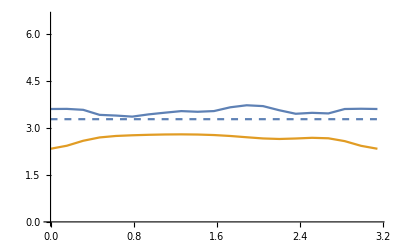

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],ListLinePlot[{tm32max,tm32mean}]]
```

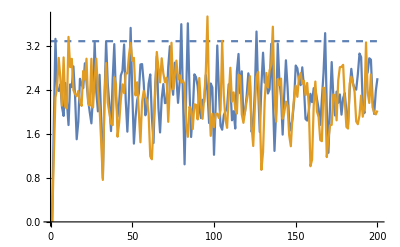

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,200},PlotStyle->Dashed],ListLinePlot[{tm32n[[1]],tm16n[[1]]}],PlotRange->All]
```

## dt = pi/64

#### data

```mathematica
tm64={-0.000000000000000000*10^+00,1.944736965868449463*10^+00,3.812072498911429630*10^+00,2.163534400830550819*10^+00,9.272042370577886494*10^-01,2.001114414554166832*10^+00,2.875934042263190271*10^+00,2.131016407236393739*10^+00,2.018202314286245524*10^+00,2.655573672428946264*10^+00,2.942361855225029021*10^+00,2.059690972903935435*10^+00,1.039068111785644843*10^+00,2.296282689967191093*10^+00,3.607593672843954824*10^+00,2.182610669119554814*10^+00,7.388406519903123471*10^-01,2.070923169260709074*10^+00,3.339179847313528349*10^+00,2.341700470359846076*10^+00,1.840835331109556883*10^+00,2.072208692459676538*10^+00,2.412253098228896331*10^+00,2.291275331435960183*10^+00,2.715695699887914039*10^+00,2.399616262400962263*10^+00,2.004292521145592421*10^+00,2.131313310862258614*10^+00,2.086190169351980650*10^+00,2.406428527897707337*10^+00,2.633786567779607068*10^+00,2.198225014668781618*10^+00,1.815188943927892762*10^+00,2.242292836636459619*10^+00,2.437573759964441589*10^+00,2.350559275638135492*10^+00,2.847607809588296401*10^+00,2.197328625118716516*10^+00,1.816677541059700030*10^+00,2.367567733352484272*10^+00,3.339625629045032351*10^+00,2.201950934831880424*10^+00,1.109151657255728063*10^+00,2.074395775508538708*10^+00,2.992337221909568967*10^+00,2.353782656165577691*10^+00,1.474293470176591736*10^+00,1.978426288074235595*10^+00,2.581495557273448593*10^+00,2.738463966136207350*10^+00,2.140068747976216823*10^+00,2.144044011947035422*10^+00,2.738240925223890621*10^+00,2.672241385421092907*10^+00,2.134064042279775641*10^+00,2.292381848604194694*10^+00,3.089713147622803469*10^+00,2.352201767962382117*10^+00,1.186899559262730053*10^+00,1.929499904860060955*10^+00,3.056196185778291774*10^+00,2.536616064995574238*10^+00,1.182828009422252302*10^+00,1.906802975329539462*10^+00,3.338543033626921286*10^+00,2.425542786950090957*10^+00,1.060709812301737109*10^+00,2.006098886981204199*10^+00,3.611816237024619181*10^+00,2.437879038282440902*10^+00,1.218775644623228072*10^+00,2.138618389476562243*10^+00,3.413675840206184642*10^+00,2.252945693595798105*10^+00,9.879788600973102852*10^-01,2.015300250306141461*10^+00,3.427400602387528750*10^+00,2.013598433650042985*10^+00,7.856184851281112769*10^-01,1.935047178408288993*10^+00,3.288409014027463773*10^+00,2.360132329529176065*10^+00,1.433619346176958409*10^+00,1.969051269720576425*10^+00,3.058075331468761426*10^+00,2.629092314794273300*10^+00,1.855014984170268999*10^+00,2.217323703193476714*10^+00,2.850088657941952874*10^+00,2.112337606527023404*10^+00,1.759942051204075097*10^+00,2.303367834965764249*10^+00,2.986351797045574852*10^+00,1.918276641721531783*10^+00,1.571014510745108339*10^+00,2.606851935497036976*10^+00,3.130399149623376953*10^+00,1.788898473700789804*10^+00,1.647228322618305318*10^+00,2.756152082976778050*10^+00,2.829869100138992621*10^+00,2.000910286169497621*10^+00,1.991622704884385309*10^+00,2.778499909712011551*10^+00,2.461017606117168466*10^+00,1.708539621223907012*10^+00,2.107608148427402739*10^+00,2.997128606594704259*10^+00,2.474393229064006494*10^+00,1.434185348733604926*10^+00,1.868117976823590043*10^+00,3.237762526848695366*10^+00,2.476439893394944747*10^+00,1.257077691621037774*10^+00,1.854811321258166057*10^+00,3.226841477884118348*10^+00,2.311289038663049578*10^+00,1.452213416327668760*10^+00,2.108468999545382694*10^+00,3.082317380652300542*10^+00,2.321318492283132251*10^+00,1.660491167552920810*10^+00,2.513500528066102468*10^+00,3.420744199527105955*10^+00,2.173764871006904631*10^+00,1.308747837486795351*10^+00,2.373612295180608900*10^+00,3.489972202731788986*10^+00,1.876507468065967021*10^+00,1.115000184228824853*10^+00,2.398598128415341701*10^+00,3.259555157813792459*10^+00,1.808061498704187198*10^+00,1.176476188060180839*10^+00,2.351594622665763357*10^+00,3.165771000215539921*10^+00,2.167672793009022492*10^+00,1.856856935889273030*10^+00,2.824248021655393348*10^+00,3.098719693826655242*10^+00,1.964349869757316736*10^+00,1.565916705484956761*10^+00,2.729110816277058760*10^+00,3.076132588548716740*10^+00,1.806335236380958609*10^+00,8.512384649075122045*10^-01,2.267945221235434961*10^+00,3.318054459386272637*10^+00,1.931848752747438835*10^+00,6.909220820975600086*10^-01,2.073888632891697448*10^+00,3.485465226851958587*10^+00,2.290934330346025671*10^+00,1.465800590177591678*10^+00,2.250481820574273595*10^+00,3.256144348208431349*10^+00,2.242689840660266221*10^+00,1.841270296450780330*10^+00,2.401349901876423942*10^+00,2.534984317880416782*10^+00,2.170987370608015166*10^+00,1.939135147844767593*10^+00,2.395118264202818814*10^+00,2.623693657683018987*10^+00,2.108089188478877496*10^+00,1.482780261289939006*10^+00,2.195751021859225993*10^+00,3.026914603142405902*10^+00,2.359527649505680724*10^+00,2.147479116647034836*10^+00,2.080941991482216480*10^+00,2.336824558050059508*10^+00,2.375396454011963865*10^+00,2.903147446415314192*10^+00,2.272650448412724344*10^+00,1.513698371496588146*10^+00,2.257010537164877650*10^+00,3.043500838634569661*10^+00,2.458349281700340505*10^+00,1.751335062443217794*10^+00,2.199842811960084354*10^+00,2.482845572979982762*10^+00,2.597887597819249272*10^+00,2.511735460763988126*10^+00,2.359273820852261228*10^+00,2.804012956484155161*10^+00,2.164115029052672501*10^+00,1.466450712187839178*10^+00,2.348500705693950863*10^+00,3.651903008152492358*10^+00,2.078426608862320890*10^+00,3.984538432687825260*10^-01,2.067862293624632919*10^+00,3.606151912136054349*10^+00,2.231078760847204023*10^+00,9.510886060970524802*10^-01,1.864112748404390452*10^+00,2.729397005142628618*10^+00,2.675314441747977945*10^+00,1.959518959564838791*10^+00,2.722912528242654327*10^-14,1.944075957452446435*10^+00,3.810559684492280219*10^+00,2.409211748990385260*10^+00,1.221784065004215769*10^+00,2.244166889291898670*10^+00,2.976067834205315954*10^+00,2.218694246167951523*10^+00,2.022645587973305847*10^+00,2.656106294146306723*10^+00,2.979028713564283670*10^+00,2.268567177479416941*10^+00,1.338954837487640326*10^+00,2.518468534880716980*10^+00,3.478744944683248352*10^+00,2.086509870209027895*10^+00,7.655539958833432745*10^-01,2.071335919307286666*10^+00,3.328305628784519854*10^+00,2.476296529295249016*10^+00,2.052841917136641214*10^+00,2.227904371782550186*10^+00,2.504428909592749886*10^+00,2.365912536371738817*10^+00,2.686308970173537425*10^+00,2.407504430860476496*10^+00,2.093320600694247968*10^+00,2.247372053588170715*10^+00,2.270182845538822214*10^+00,2.489261058109192959*10^+00,2.596906231414684907*10^+00,2.123150052261515874*10^+00,1.807484131548471096*10^+00,2.249766348403109184*10^+00,2.452205118257742900*10^+00,2.436725945347960387*10^+00,2.949036022949372171*10^+00,2.383428022051028439*10^+00,2.005842922647923743*10^+00,2.482149560046939651*10^+00,3.287526375636864895*10^+00,2.235935454440383108*10^+00,1.223877913742650314*10^+00,2.105671897637392931*10^+00,3.009418173015025566*10^+00,2.450586448682316565*10^+00,1.592787513557306411*10^+00,1.985027965162331931*10^+00,2.589420757336206247*10^+00,2.735982272511420899*10^+00,2.184946900992412733*10^+00,2.258383592135598583*10^+00,2.889630345239862397*10^+00,2.806571363818340714*10^+00,2.280204502783027998*10^+00,2.358339158217766851*10^+00,3.067068457069012766*10^+00,2.408744155095664308*10^+00,1.318713990327462060*10^+00,2.021920553789074315*10^+00,3.115026581686142659*10^+00,2.712249187939396400*10^+00,1.420147110055026696*10^+00,2.039165356937071127*10^+00,3.272516260165694746*10^+00,2.399990707003859747*10^+00,1.128951838206556868*10^+00,2.073831670819042294*10^+00,3.627439213581195698*10^+00,2.672689430500748475*10^+00,1.489535468607360524*10^+00,2.318153486358427884*10^+00,3.303188458498838020*10^+00,2.231653594177763544*10^+00,1.037339260545227626*10^+00,2.059914261264919055*10^+00,3.428499810919271695*10^+00,2.212655196005778535*10^+00,1.124435584619553730*10^+00,2.179845797447677036*10^+00,3.177207857365092813*10^+00,2.260506510985799355*10^+00,1.414181204824474847*10^+00,2.018641093664650388*10^+00,3.096605198859210706*10^+00,2.801374318330214663*10^+00,2.096229861888275092*10^+00,2.378071220517069762*10^+00,2.797596804437207041*10^+00,2.088189671183230178*10^+00,1.766844466370119271*10^+00,2.363538472158464465*10^+00,3.069862454795981854*10^+00,2.128817809308226394*10^+00,1.870969522118592021*10^+00,2.834114281493634646*10^+00,2.991310409334956510*10^+00,1.645025694999617594*10^+00,1.584366310985325876*10^+00,2.704910203098552568*10^+00,2.901236602630127948*10^+00,2.212347968558322719*10^+00,2.230716589840518349*10^+00,2.861377543130864787*10^+00,2.420843680287502853*10^+00,1.666569773865048232*10^+00,2.086467771313700315*10^+00,2.980547988788164737*10^+00,2.622637639377631391*10^+00,1.670472691283912514*10^+00,2.157911543341789695*10^+00,3.350210996706060484*10^+00,2.418233831328818972*10^+00,1.156124186211924698*10^+00,1.830183239387836114*10^+00,3.146856283879049254*10^+00,2.422387492810107901*10^+00,1.681593678648835910*10^+00,2.336154178739008103*10^+00,3.162552299796048239*10^+00,2.352858365926561390*10^+00,1.643491939110611089*10^+00,2.477815344309192369*10^+00,3.361017970974978564*10^+00,2.321351867644096512*10^+00,1.533739280081655831*10^+00,2.575404363496935467*10^+00,3.514381465519631487*10^+00,1.977243320434313389*10^+00,1.103905987472493244*10^+00,2.350703931051286055*10^+00,3.176249165375255146*10^+00,1.973132289235641323*10^+00,1.409384698747480069*10^+00,2.495655994481973394*10^+00,3.199365293718406278*10^+00,2.291813572074500982*10^+00,1.939024892016833368*10^+00,2.769453610081777928*10^+00,3.033986157170206255*10^+00,2.055625579396561431*10^+00,1.780137103692373879*10^+00,2.794768745334188953*10^+00,3.117368798449065892*10^+00,1.983358366635586290*10^+00,1.041665124265445330*10^+00,2.331583143366111166*10^+00,3.278216173106986098*10^+00,2.101179968646384566*10^+00,9.813264661549659928*10^-01,2.303166070782235231*10^+00,3.455507729044228427*10^+00,2.346498135740883839*10^+00,1.602850567602842169*10^+00,2.244653172613458647*10^+00,3.123488304714023389*10^+00,2.271136853741440920*10^+00,1.986068125775757087*10^+00,2.506518515043115070*10^+00,2.653622885665980924*10^+00,2.345450881179643510*10^+00,2.127180964322628487*10^+00,2.423622050994548083*10^+00,2.563340981908050153*10^+00,2.166836248946254706*10^+00,1.669763890278182616*10^+00,2.348651905328813960*10^+00,3.036429312683615489*10^+00,2.451995860868579236*10^+00,2.249997885812739185*10^+00,2.081750771131538613*10^+00,2.203249809714049157*10^+00,2.319340467352139612*10^+00,2.916095535361419966*10^+00,2.463128578498794852*10^+00,1.727965066615022138*10^+00,2.473076169181303463*10^+00,3.168710353101094945*10^+00,2.443744403431797885*10^+00,1.630573261988307099*10^+00,2.163839707626586506*10^+00,2.523749609408674210*10^+00,2.730976811423921458*10^+00,2.610044542509075693*10^+00,2.509326976966621547*10^+00,2.847827102670353661*10^+00,2.175291637728238303*10^+00,1.425262369175573252*10^+00,2.333191350476579107*10^+00,3.647944608891655172*10^+00,2.311581199574479051*10^+00,6.643841826182159682*10^-01,2.313783361988019038*10^+00,3.673517082780310083*10^+00,2.252701049378615927*10^+00,9.196608681862458168*10^-01,1.844339538540603618*10^+00,2.709511345407818350*10^+00,2.739039357267355701*10^+00,2.115767180271827641*10^+00,-9.610279511444755881*10^-16,1.942157932817172306*10^+00,3.806230320042755189*10^+00,2.752646785499249127*10^+00,1.697769524517165785*10^+00,2.614735170284483434*10^+00,3.120626194621868077*10^+00,2.356448558331868171*10^+00,2.006399166869548445*10^+00,2.667929583063577414*10^+00,3.052437888591267079*10^+00,2.565647777793277573*10^+00,1.861084504845234688*10^+00,2.896457117682414761*10^+00,3.144151419872315945*10^+00,1.851418070602523613*10^+00,7.861911650122132000*10^-01,2.076046622158303823*10^+00,3.315219944756480075*10^+00,2.637568452493859184*10^+00,2.399546259583056340*10^+00,2.574144218314150301*10^+00,2.648730652474911018*10^+00,2.417322221238689117*10^+00,2.556108828699573454*10^+00,2.427377493495347593*10^+00,2.310314615069605448*10^+00,2.405932550696554095*10^+00,2.524368123423402110*10^+00,2.706547326423354161*10^+00,2.472949526108980223*10^+00,1.935130496529625654*10^+00,1.815319218174272331*10^+00,2.275031629274002487*10^+00,2.517295476364235896*10^+00,2.541926515778423212*10^+00,3.121786042278783313*10^+00,2.771364923958127946*10^+00,2.293494479931195595*10^+00,2.546103699826812949*10^+00,3.124029367211549335*10^+00,2.308581601632111013*10^+00,1.535594535216350920*10^+00,2.176962428074855627*10^+00,3.028132592760838904*10^+00,2.651863319311247302*10^+00,1.788132575874667785*10^+00,1.947536607237327910*10^+00,2.571069958456411619*10^+00,2.722680968721429728*10^+00,2.310154964024960567*10^+00,2.423518337154158431*10^+00,3.104249609142393673*10^+00,3.049317007886477526*10^+00,2.472051281939061429*10^+00,2.376291033041113998*10^+00,2.996130641574425102*10^+00,2.507488055626081014*10^+00,1.593881081608646166*10^+00,2.231732888490642885*10^+00,3.233872859235524366*10^+00,3.014480446949560299*10^+00,1.809974654262301641*10^+00,2.266749558543609044*10^+00,3.090184997284549873*10^+00,2.326809619243578098*10^+00,1.267730292805816728*10^+00,2.196156723610207528*10^+00,3.642515628836586750*10^+00,3.011584170766256729*10^+00,1.894214370280562054*10^+00,2.578976699815608953*10^+00,3.029266109105090976*10^+00,2.165658803421799394*10^+00,1.181110141234184674*10^+00,2.173648361052770372*10^+00,3.431759192054065100*10^+00,2.508101288422718511*10^+00,1.673681172724967858*10^+00,2.637059608980337089*10^+00,2.898979196525012014*10^+00,1.990316763847750137*10^+00,1.360154254254850592*10^+00,2.130850182563891693*10^+00,3.180906681739492647*10^+00,2.993897263249742480*10^+00,2.439400677997551448*10^+00,2.699598954400754813*10^+00,2.677586663374869058*10^+00,2.014919881572944327*10^+00,1.809941668206910048*10^+00,2.524957968721551538*10^+00,3.239722061527494201*10^+00,2.426279966364398355*10^+00,2.305469128557042779*10^+00,3.250752005671028400*10^+00,2.650834605655467691*10^+00,1.267829109068034033*10^+00,1.418720493627586343*10^+00,2.572690067308068151*10^+00,3.038394938150258184*10^+00,2.440942271012759068*10^+00,2.576860655158943469*10^+00,3.088841937203345545*10^+00,2.368507904857201751*10^+00,1.579076669288866919*10^+00,2.070553723587619022*10^+00,2.984173919024227573*10^+00,2.871575216899186156*10^+00,1.979553582891975250*10^+00,2.604932426684594571*10^+00,3.587640241266651042*10^+00,2.284625198449632855*10^+00,9.147027593989898175*10^-01,1.711190310080632937*10^+00,2.939474849283631119*10^+00,2.612957015271127670*10^+00,2.015881796140716276*10^+00,2.674209447285885055*10^+00,3.327135696249977848*10^+00,2.413539239215214849*10^+00,1.614724439792344368*10^+00,2.402429994736519969*10^+00,3.232558483908608338*10^+00,2.595094534576681156*10^+00,1.894360710347883447*10^+00,2.912215300317546163*10^+00,3.558677291337796422*10^+00,2.149730266975653503*10^+00,1.161814795728804528*10^+00,2.226772383606411054*10^+00,2.951869263602649784*10^+00,2.195364118659315356*10^+00,1.847505078456597616*10^+00,2.763653692387287197*10^+00,3.269287570141611976*10^+00,2.480569040173106199*10^+00,2.119225611446160951*10^+00,2.636375679350162482*10^+00,2.876514122042428845*10^+00,2.207616025974637353*10^+00,2.156666405341613579*10^+00,2.952431835915823477*10^+00,3.159825107521497589*10^+00,2.224376428563660024*10^+00,1.483915118362732155*10^+00,2.424887221936736559*10^+00,3.151203924861590622*10^+00,2.340346004386004264*10^+00,1.567788347784349945*10^+00,2.699106513128966434*10^+00,3.393623953086051692*10^+00,2.466571685521081303*10^+00,1.916702773488571099*10^+00,2.239450959294550181*10^+00,2.803290592631982658*10^+00,2.299424206731763842*10^+00,2.280980020491845117*10^+00,2.775687077078291765*10^+00,2.786252756567730859*10^+00,2.565377201201895385*10^+00,2.522872355301365221*10^+00,2.502913587840924325*10^+00,2.398176647741601109*10^+00,2.234050715354851668*10^+00,2.059178251929506320*10^+00,2.673779613047571058*10^+00,3.036198943758483981*10^+00,2.584046027495706888*10^+00,2.534152781089579864*10^+00,2.095194228120262014*10^+00,1.876610387612696496*10^+00,2.204919112749692989*10^+00,2.962302563585131665*10^+00,2.796201015360928466*10^+00,1.950613374613213713*10^+00,2.728108965665776431*10^+00,3.410748302769130103*10^+00,2.406587610311814451*10^+00,1.386276415290053521*10^+00,2.064784878089502396*10^+00,2.606815827523342399*10^+00,2.984914307267839462*10^+00,2.685142376133388797*10^+00,2.747634372544822678*10^+00,2.976391772879089626*10^+00,2.233701648144232887*10^+00,1.341362266668795211*10^+00,2.307931819059768408*10^+00,3.651103256028717325*10^+00,2.661733568046774412*10^+00,1.042905582482782201*10^+00,2.670885675854554275*10^+00,3.785108444797165017*10^+00,2.300187347210055577*10^+00,9.463704996841303396*10^-01,1.797130500939120967*10^+00,2.638117327344858154*10^+00,2.839397583116254786*10^+00,2.324755447236491968*10^+00,9.610279511444749964*10^-16,1.939171418525548418*10^+00,3.799654031364017470*10^+00,2.951714597167753862*10^+00,2.085697385472795151*10^+00,2.943441555561742362*10^+00,3.147377628795023696*10^+00,2.327458289754297915*10^+00,1.927772803480426678*10^+00,2.699552891358185214*10^+00,3.167541758195283386*10^+00,2.707909670393904289*10^+00,2.269395022479246737*10^+00,3.221884431038069430*10^+00,2.734172619591402675*10^+00,1.514607403160227017*10^+00,7.907532809234129045*10^-01,2.090547888178059477*10^+00,3.330459931848821942*10^+00,2.678270804030942642*10^+00,2.658152815934488267*10^+00,2.914278604547060780*10^+00,2.706543838901340315*10^+00,2.292557213528040982*10^+00,2.357019279950505641*10^+00,2.455123555095164445*10^+00,2.524420247655218663*10^+00,2.456472711491775485*10^+00,2.671254958100891752*10^+00,2.918928788710343447*10^+00,2.308585544020362423*10^+00,1.645583093980514278*10^+00,1.771460778972116179*10^+00,2.306210374491645787*10^+00,2.642006372508493239*10^+00,2.556147971773358396*10^+00,3.216619489374034746*10^+00,3.130124073768157267*10^+00,2.482538774775950863*10^+00,2.407960796333342479*10^+00,2.847130294645905391*10^+00,2.387432920262908098*10^+00,1.842809539537008767*10^+00,2.242301338279736544*10^+00,2.990840768631422897*10^+00,2.845381964653920903*10^+00,1.979354244238725968*10^+00,1.870146797687590512*10^+00,2.496520971217667473*10^+00,2.668789882111591183*10^+00,2.413262022143685126*10^+00,2.526664088918213036*10^+00,3.222582003630080294*10^+00,3.236361200629776391*10^+00,2.594454331699532545*10^+00,2.299289434829868917*10^+00,2.835748983203765228*10^+00,2.593622559211318013*10^+00,1.845061373837451058*10^+00,2.425443569984337522*10^+00,3.325706446341627043*10^+00,3.204262421024535623*10^+00,2.166680362709079599*10^+00,2.477314485204368921*10^+00,2.832594337736481727*10^+00,2.201230679701601911*10^+00,1.385327075050830414*10^+00,2.312939565337734482*10^+00,3.621220163353068511*10^+00,3.191212264668805254*10^+00,2.208924108510851525*10^+00,2.726825939995281445*10^+00,2.748532397209901834*10^+00,2.085824658835069290*10^+00,1.344941001334289066*10^+00,2.333615230357576120*10^+00,3.448145475636851920*10^+00,2.642111770657522563*10^+00,2.100987769883947642*10^+00,3.052214623074649857*10^+00,2.581206861773877925*10^+00,1.623424881887600479*10^+00,1.292939664014848278*10^+00,2.233152512602618156*10^+00,3.256960206924184753*10^+00,3.021018336311558361*10^+00,2.646153011304627434*10^+00,2.977246273523972420*10^+00,2.588646715684584709*10^+00,1.920558512861538336*10^+00,1.891498003392595217*10^+00,2.694359776424183561*10^+00,3.390016793816743146*10^+00,2.536301505493713915*10^+00,2.599392329147721448*10^+00,3.614011190730582523*10^+00,2.270944731628168789*10^+00,8.053636184581484114*10^-01,1.211123530686567751*10^+00,2.408658007687926705*10^+00,3.138093944834229987*10^+00,2.549836659758709878*10^+00,2.798245073651659531*10^+00,3.285772828958327452*10^+00,2.377270455786137049*10^+00,1.509985142169531391*10^+00,2.107092395589945877*10^+00,3.018204103666537019*10^+00,3.051388220791016792*10^+00,2.150990197256048564*10^+00,2.898699328176461698*10^+00,3.771316121723374160*10^+00,2.164766681693103934*10^+00,7.060536381650317495*10^-01,1.549580760148085989*10^+00,2.675602057224628183*10^+00,2.712598382347554349*10^+00,2.254388363976737253*10^+00,2.896519840590402683*10^+00,3.428341734492454496*10^+00,2.492946262411376512*10^+00,1.680393626937866092*10^+00,2.356041962263254241*10^+00,3.127222912556049561*10^+00,2.769995072511362011*10^+00,2.206135949110014760*10^+00,3.131413860614871592*10^+00,3.549595014632435319*10^+00,2.311199835250207890*10^+00,1.292165487614088448*10^+00,2.081781834603804171*10^+00,2.682667208889985666*10^+00,2.337329213059645916*10^+00,2.270222793102524950*10^+00,2.961172082948330342*10^+00,3.260275753471223226*10^+00,2.610563318079780259*10^+00,2.330042202449016386*10^+00,2.534069277865429903*10^+00,2.718329398247457451*10^+00,2.297041342277737819*10^+00,2.473338706697107980*10^+00,3.089553760677053784*10^+00,3.129957327135612477*10^+00,2.355864789246723490*10^+00,1.902222716196991792*10^+00,2.506934841077821829*10^+00,2.952422624949068819*10^+00,2.479078757609932904*10^+00,2.117619485751127684*10^+00,3.047216773783113730*10^+00,3.294724971497684951*10^+00,2.545866650870292069*10^+00,2.296034005408165157*10^+00,2.279461600736649718*10^+00,2.460401483499949471*10^+00,2.289665756775234762*10^+00,2.566788167274764110*10^+00,3.047925642810511704*10^+00,2.755628498819117755*10^+00,2.632620474042171921*10^+00,2.892693551055841805*10^+00,2.592569229206662218*10^+00,2.173256437556092102*10^+00,2.234929620294699326*10^+00,2.400334642506037675*10^+00,2.961548742254906053*10^+00,2.937379898865898564*10^+00,2.663600477375278608*10^+00,2.831290218271879322*10^+00,2.162065259935780137*10^+00,1.590494080494151197*10^+00,2.104104090694590923*10^+00,3.015246308900053407*10^+00,3.098919284789467099*10^+00,2.008039666130732925*10^+00,2.833160500495721656*10^+00,3.582358693034183084*10^+00,2.405887029235060481*10^+00,1.147888495839648026*10^+00,1.955632043446922985*10^+00,2.697654494357383470*10^+00,3.199402039013198973*10^+00,2.649913792291009429*10^+00,2.930997292645156627*10^+00,3.135409883074613546*10^+00,2.332714334044671212*10^+00,1.371261631257266966*10^+00,2.289653464049868692*10^+00,3.600128518095033758*10^+00,2.916906192223557959*10^+00,1.446367791647269252*10^+00,2.913845847645758713*10^+00,3.807156153209905192*10^+00,2.354934010423792579*10^+00,1.097810711838842268*10^+00,1.790642571642720338*10^+00,2.576557775576815867*10^+00,2.873799150631553889*10^+00,2.456455792336389887*10^+00,4.805139755722374982*10^-16,1.935409717537414309*10^+00,3.791621080934651555*10^+00,2.926453344581472660*10^+00,2.295257557397363257*10^+00,3.199610155430431924*10^+00,3.061117818815286107*10^+00,2.090043191563756952*10^+00,1.780333227660000572*10^+00,2.776317574744055161*10^+00,3.271054760244545889*10^+00,2.654968743523168584*10^+00,2.490101955473207340*10^+00,3.456319478110763121*10^+00,2.390025700225225869*10^+00,1.141915262938432374*10^+00,7.704307442471833856*10^-01,2.114893544029863293*10^+00,3.378385796006504016*10^+00,2.612488625556366628*10^+00,2.771342074216032625*10^+00,3.251125630574019709*10^+00,2.710471731764487746*10^+00,1.997755577405977645*10^+00,2.107858103746238942*10^+00,2.495719733445947330*10^+00,2.687009424594381635*10^+00,2.426738869871558624*10^+00,2.683067652586676566*10^+00,3.092596907459860489*10^+00,2.227248817588177499*10^+00,1.362206837241250135*10^+00,1.671178754418852552*10^+00,2.319048335879962064*10^+00,2.758134104592158575*10^+00,2.511763255143069085*10^+00,3.219180720848596078*10^+00,3.357365692886212560*10^+00,2.586058035066509220*10^+00,2.152903216254193897*10^+00,2.524210622980269214*10^+00,2.428941509598467885*10^+00,2.084100049977755997*10^+00,2.315070706569096082*10^+00,2.936588208502313613*10^+00,2.959242339312660341*10^+00,2.217163115707180943*10^+00,1.909069662919073318*10^+00,2.372378949541243731*10^+00,2.571852078110314466*10^+00,2.471106817801759892*10^+00,2.615420667827835111*10^+00,3.244137988022020469*10^+00,3.291439830529899080*10^+00,2.672038513837565521*10^+00,2.264175270767781800*10^+00,2.628094437078313028*10^+00,2.586442314353485372*10^+00,2.073521724529082455*10^+00,2.605821020551676526*10^+00,3.370404123498170534*10^+00,3.220548147369432623*10^+00,2.394215243573722063*10^+00,2.769584809316556040*10^+00,2.593894440713074623*10^+00,2.015752822685306977*10^+00,1.439701786856773635*10^+00,2.395116525134479701*10^+00,3.559120677665564170*10^+00,3.169774051373206447*10^+00,2.392202336287263087*10^+00,2.820888354573389822*10^+00,2.558794957603667708*10^+00,2.001464520217633325*10^+00,1.514132584614406918*10^+00,2.484520744096031741*10^+00,3.482591776988934740*10^+00,2.615289271581962005*10^+00,2.328155080467112281*10^+00,3.374569163580872555*10^+00,2.347127465380763667*10^+00,1.240673472015145995*10^+00,1.220468950555950061*10^+00,2.280435825922155324*10^+00,3.284925769715395294*10^+00,2.900318285613589175*10^+00,2.688599671462947427*10^+00,3.150026533308088350*10^+00,2.557595008488834587*10^+00,1.827758203867002162*10^+00,2.010414123764663330*10^+00,2.830637173287304353*10^+00,3.455544158245272168*10^+00,2.482304934055487688*10^+00,2.714706457626715697*10^+00,3.832716411630331610*10^+00,2.063299389052746680*10^+00,4.205045554754833215*10^-01,1.014562345376190722*10^+00,2.241403752643068792*10^+00,3.156659276778264633*10^+00,2.536249334800986688*10^+00,2.824676660533951278*10^+00,3.366873686158081913*10^+00,2.519152777912960772*10^+00,1.610971267734853996*10^+00,2.162326029747725364*10^+00,3.018212120750464411*10^+00,3.119714830516118642*10^+00,2.253556356830909380*10^+00,3.006332531550027554*10^+00,3.812063003033525188*10^+00,2.176625019291125174*10^+00,7.044478409967899202*10^-01,1.442239765135199914*10^+00,2.443932716638501645*10^+00,2.711536738304110905*10^+00,2.478612887698173672*10^+00,2.974129573605157617*10^+00,3.395267127663941231*10^+00,2.625585155575536511*10^+00,1.924269989866187025*10^+00,2.405419117785355887*10^+00,3.035627324870936228*10^+00,2.812063741693997532*10^+00,2.476400485278408503*10^+00,3.215283138685692155*10^+00,3.437549492210647095*10^+00,2.382362922515131487*10^+00,1.535584818507222060*10^+00,1.983922571796210343*10^+00,2.417654857278153990*10^+00,2.385761738998852355*10^+00,2.605826930790712481*10^+00,3.112861158309284448*10^+00,3.147348256640866371*10^+00,2.692220908154525638*10^+00,2.576489114709535677*10^+00,2.521941875108500319*10^+00,2.528616521021286978*10^+00,2.306148323979268167*10^+00,2.680551766984996753*10^+00,3.151608928911144858*10^+00,2.998537532018715090*10^+00,2.364705571293800546*10^+00,2.267146315641782373*10^+00,2.592896078555162909*10^+00,2.739188991185978139*10^+00,2.483441403495185718*10^+00,2.518195886604091882*10^+00,3.267395745162613885*10^+00,3.151270219516256965*10^+00,2.603553982523489463*10^+00,2.678365424879219248*10^+00,2.430348898728584395*10^+00,2.200034933236120427*10^+00,2.250745470511091195*10^+00,2.766679827749972453*10^+00,3.223470736246049739*10^+00,2.614422626787676229*10^+00,2.550315775090078674*10^+00,3.141264074665932604*10^+00,2.698416645509345457*10^+00,2.032470928131711929*10^+00,2.176646973499718030*10^+00,2.600275142397874273*10^+00,3.130395848218441301*10^+00,2.823159622839824578*10^+00,2.724585316889905684*10^+00,3.049592708596198687*10^+00,2.291115413236489040*10^+00,1.508560864943525814*10^+00,2.080158374346924965*10^+00,3.044183340090249157*10^+00,3.259694385578435494*10^+00,2.028446518307239543*10^+00,2.810906212759211709*10^+00,3.621509113281026426*10^+00,2.432313888513082389*10^+00,1.136833801213016137*10^+00,1.890110499306462799*10^+00,2.738538178255061073*10^+00,3.299364377151359662*10^+00,2.642026531443230297*10^+00,3.032622373599585863*10^+00,3.213197135402237503*10^+00,2.409840274551350969*10^+00,1.534596999866261635*10^+00,2.358512425469653451*10^+00,3.476619455599944342*10^+00,3.007119944943105416*10^+00,1.800889407507568318*10^+00,3.044212774979426772*10^+00,3.701669072328903631*10^+00,2.371603344699613647*10^+00,1.384246374164939564*10^+00,1.912591644727650975*10^+00,2.526984449651703990*10^+00,2.831411409495276921*10^+00,2.567059279174138009*10^+00,3.203426503814917641*10^-16,1.931241832255828239*10^+00,3.782993327322309973*10^+00,2.770537848641362988*10^+00,2.350581957381076226*10^+00,3.417548945797987070*10^+00,2.956093771991019636*10^+00,1.741108946139271918*10^+00,1.565702558626244523*10^+00,2.837183213111436064*10^+00,3.407754113546192620*10^+00,2.532948480272603220*10^+00,2.556811975649348145*10^+00,3.611545898929613863*10^+00,2.208740685226647571*10^+00,8.166473861242572463*10^-01,7.395406223829541492*10^-01,2.131506082615172382*10^+00,3.445897905376759329*10^+00,2.508375395797767471*10^+00,2.774853019152637046*10^+00,3.499843438825129383*10^+00,2.719184557032314764*10^+00,1.684241845726389908*10^+00,1.880087462868072601*10^+00,2.540733252633256889*10^+00,2.820943945454136070*10^+00,2.400556373314252312*10^+00,2.648482965356389052*10^+00,3.213636776897607739*10^+00,2.315973301477662449*10^+00,1.248288528291456645*10^+00,1.578438208941698617*10^+00,2.320459244019965617*10^+00,2.849181510758673319*10^+00,2.505332532452786864*10^+00,3.174610659343784391*10^+00,3.465823414817019721*10^+00,2.651691883385410620*10^+00,1.949485405320054099*10^+00,2.257696202024431553*10^+00,2.435807957974589488*10^+00,2.275005151179465557*10^+00,2.431461465495801555*10^+00,2.939635885358395928*10^+00,2.996499440020918836*10^+00,2.408233302501635364*10^+00,2.110894164920871674*10^+00,2.272562105434337010*10^+00,2.408949025797223698*10^+00,2.448707705069331109*10^+00,2.745768585917945259*10^+00,3.238231803826213895*10^+00,3.245250825665404459*10^+00,2.678566323839896235*10^+00,2.288431070919247023*10^+00,2.492313394327282605*10^+00,2.523026538370456429*10^+00,2.229253162986897685*10^+00,2.773166245020727949*10^+00,3.397547193210418204*10^+00,3.108372118788095495*10^+00,2.506134799941649227*10^+00,3.027630597152165759*10^+00,2.453894470907253655*10^+00,1.790920642370762872*10^+00,1.447594799915851160*10^+00,2.429936447943906064*10^+00,3.449460937509409852*10^+00,3.043898683699167940*10^+00,2.421865687954531055*10^+00,2.900803967954124651*10^+00,2.536078230799950539*10^+00,1.952427784801642030*10^+00,1.696422681813975597*10^+00,2.648683964779122046*10^+00,3.512887994187488871*10^+00,2.497692623682802093*10^+00,2.395832283691043951*10^+00,3.596757307229483835*10^+00,2.268699598726436228*10^+00,9.452013590625667483*10^-01,1.155755158367806512*10^+00,2.277221599351577197*10^+00,3.247899666229380866*10^+00,2.746221732705140361*10^+00,2.605942102119484627*10^+00,3.204541245428793594*10^+00,2.706680605981774068*10^+00,1.893069105745895708*10^+00,2.103351988750200796*10^+00,2.904225974399619048*10^+00,3.447403942606532823*10^+00,2.418039411207235645*10^+00,2.746809128729693406*10^+00,3.909247490388141788*10^+00,2.014922325333877495*10^+00,2.805259889119942618*10^-01,9.328956596469775153*10^-01,2.131920808802485023*10^+00,3.105503877077064878*10^+00,2.553833127165089589*10^+00,2.776529591900032123*10^+00,3.339447054000980408*10^+00,2.740970133554514021*10^+00,1.915288932799162236*10^+00,2.258604432487512970*10^+00,2.962466568883280527*10^+00,3.118015083483495431*10^+00,2.448063173945937088*10^+00,3.046914774107542634*10^+00,3.727157140708027505*10^+00,2.235618650773146587*10^+00,9.061824608132409420*10^-01,1.444539365769535788*10^+00,2.266737784412645951*10^+00,2.661938204464266988*10^+00,2.700618166564318745*10^+00,3.031159142552431796*10^+00,3.269574222954048537*10^+00,2.773656824577525271*10^+00,2.294294896184791543*10^+00,2.555838890280049291*10^+00,2.926836294624050261*10^+00,2.776835162407774504*10^+00,2.689635517987778002*10^+00,3.236097795020294043*10^+00,3.268361640042066085*10^+00,2.383629202522329571*10^+00,1.779015922784194847*10^+00,2.044066615445810697*10^+00,2.231808109004215446*10^+00,2.385071224973127180*10^+00,2.839896251780586134*10^+00,3.245642975053845802*10^+00,3.020575471680235324*10^+00,2.736204863203926863*10^+00,2.831285660796088344*10^+00,2.612105565118496564*10^+00,2.387492680046279236*10^+00,2.269833849680721105*10^+00,2.781239170785660519*10^+00,3.170266122890443405*10^+00,2.828010274252725775*10^+00,2.292983402158844441*10^+00,2.550862664666764701*10^+00,2.715570966107575313*10^+00,2.555355849249717703*10^+00,2.429892492661075210*10^+00,2.755316049289614266*10^+00,3.359023513691294927*10^+00,3.016935692563988969*10^+00,2.687695857956326595*10^+00,2.994739086677394191*10^+00,2.629700674726403342*10^+00,2.062672060617900094*10^+00,2.221164140339341841*10^+00,2.863249527431877439*10^+00,3.313844128456084448*10^+00,2.471986419901853083*10^+00,2.437968444694158077*10^+00,3.265835707051869985*10^+00,2.814845607695443341*10^+00,2.035009597185628571*10^+00,2.158345740338442287*10^+00,2.690134457355443320*10^+00,3.170124881627845781*10^+00,2.780214453950039299*10^+00,2.806065030247291148*10^+00,3.179356951555595501*10^+00,2.422957095333996058*10^+00,1.665851500377607763*10^+00,2.162791410323375185*10^+00,3.039023168312841250*10^+00,3.297146202882661026*10^+00,2.148135818329560465*10^+00,2.801023015047379161*10^+00,3.564075975782236227*10^+00,2.458398563277408577*10^+00,1.342128979311845605*10^+00,1.948604261699640183*10^+00,2.736022711130948082*10^+00,3.284863715778588933*10^+00,2.749055690132562457*10^+00,3.121322072050818797*10^+00,3.206604951120289648*10^+00,2.419750547355442372*10^+00,1.746064257866905445*10^+00,2.501903473460697747*10^+00,3.317680961947460094*10^+00,2.978917510285039150*10^+00,2.094628886065360795*10^+00,3.110124868890172145*10^+00,3.519947588495718538*10^+00,2.354091475689850999*10^+00,1.664123220661977820*10^+00,2.141344730330720481*10^+00,2.565612734146954566*10^+00,2.811078652224935137*10^+00,2.727478087601618917*10^+00,-9.610279511444755881*10^-16,1.927076045491424416*10^+00,3.774604929162316047*10^+00,2.567856662296363890*10^+00,2.329603737505793859*10^+00,3.594034399375760636*10^+00,2.917457583137284427*10^+00,1.408965559324535155*10^+00,1.371387202288758989*10^+00,2.884859227255861303*10^+00,3.504690222162949009*10^+00,2.408517177541301457*10^+00,2.547770120779399683*10^+00,3.694057503651863250*10^+00,2.196814244662129934*10^+00,6.142787742236361925*10^-01,7.170752072437429625*10^-01,2.155731605809826590*10^+00,3.522721689553717006*10^+00,2.457912760040676492*10^+00,2.731032192298014305*10^+00,3.651369052420674777*10^+00,2.751199336541905183*10^+00,1.463673657193051536*10^+00,1.705603285401739555*10^+00,2.619533788802797858*10^+00,3.006278818652268647*10^+00,2.428113573139706549*10^+00,2.629126605653727466*10^+00,3.297992242421319276*10^+00,2.446498954265020842*10^+00,1.325461734213239096*10^+00,1.540598456450766429*10^+00,2.303051218432024871*10^+00,2.916689480617266739*10^+00,2.596278976866186916*10^+00,3.119219055355977321*10^+00,3.453711108693120480*10^+00,2.664361358832060489*10^+00,1.894230991710925238*10^+00,2.082780385623820951*10^+00,2.424564835631436210*10^+00,2.455928448609340897*10^+00,2.604017907894207173*10^+00,2.999234016270230452*10^+00,3.001848023160048395*10^+00,2.552931608627361459*10^+00,2.371110971744262663*10^+00,2.283166638427394979*10^+00,2.243455525938468753*10^+00,2.414127608393591196*10^+00,2.845674744488127850*10^+00,3.234649527496812560*10^+00,3.153011309716244437*10^+00,2.611035567302318228*10^+00,2.315260899280227935*10^+00,2.462048305715194729*10^+00,2.425483565914959172*10^+00,2.351101881724657616*10^+00,2.897097369437223957*10^+00,3.409329936892078194*10^+00,2.947691334331794977*10^+00,2.539526267504442991*10^+00,3.236514240465504955*10^+00,2.451896305854823321*10^+00,1.565751587858380756*10^+00,1.412218443414770208*10^+00,2.451195163223781837*10^+00,3.317095313899851128*10^+00,2.895517674756346693*10^+00,2.390180190549853201*10^+00,2.930987056230971888*10^+00,2.644256385647549834*10^+00,2.008424120095664733*10^+00,1.854406733366938731*10^+00,2.791944477891942000*10^+00,3.529483433442367257*10^+00,2.390282434410776702*10^+00,2.393166466923682734*10^+00,3.726506830409098470*10^+00,2.296149802982517585*10^+00,7.812068435362473640*10^-01,1.107084103793134933*10^+00,2.232338603578867264*10^+00,3.166939459510154098*10^+00,2.676054148633566498*10^+00,2.486168934962432076*10^+00,3.163360198266510270*10^+00,2.888726752103204731*10^+00,2.125399447897469152*10^+00,2.200572726256210476*10^+00,2.921415312993871360*10^+00,3.425920718555080846*10^+00,2.498589701824947440*10^+00,2.773774042453331035*10^+00,3.886012388147987551*10^+00,2.067456868083022314*10^+00,3.981335195643815328*10^-01,9.294695229402639702*10^-01,2.051761376094656253*10^+00,3.029824639640476658*10^+00,2.642182750156633730*10^+00,2.739009151377091555*10^+00,3.254583436156099019*10^+00,2.938149715962228292*10^+00,2.277043121465732067*10^+00,2.361363189877068613*10^+00,2.873889990689660223*10^+00,3.100873587803959275*10^+00,2.629916123290489516*10^+00,3.095426266362533596*10^+00,3.581207277443871462*10^+00,2.252589262601365050*10^+00,1.160326562059164512*10^+00,1.574149112975929077*10^+00,2.178672941150539444*10^+00,2.640583873588502772*10^+00,2.868058773477823120*10^+00,3.103445219315774217*10^+00,3.147298945979175588*10^+00,2.925657259893529982*10^+00,2.687786891428673108*10^+00,2.744882889929385783*10^+00,2.794209608362923980*10^+00,2.727882570369402959*10^+00,2.838410946811578128*10^+00,3.252459772612548150*10^+00,3.095774958763237716*10^+00,2.341116767818133937*10^+00,1.989636087161757105*10^+00,2.202458839292384951*10^+00,2.214156490781520326*10^+00,2.411375938098277771*10^+00,2.978426276267623685*10^+00,3.327773596128461353*10^+00,2.972134456644970779*10^+00,2.825845581441650545*10^+00,3.041150947469005494*10^+00,2.751746667178084138*10^+00,2.313880796111345450*10^+00,2.247094641913398583*10^+00,2.820963212125937591*10^+00,3.169879474491755555*10^+00,2.690842380937824796*10^+00,2.213565657439334533*10^+00,2.728949434765825632*10^+00,2.842894654602045268*10^+00,2.488603083623409429*10^+00,2.385703310136059407*10^+00,2.891762500896486454*10^+00,3.377953636948393790*10^+00,2.964065008804295687*10^+00,2.821827027435433344*10^+00,3.211887778094287160*10^+00,2.827762366788634907*10^+00,2.107203477820784876*10^+00,2.215781060643306155*10^+00,2.876305018775819455*10^+00,3.339854162647951874*10^+00,2.450072397639358357*10^+00,2.384318809645186832*10^+00,3.305127339423554744*10^+00,2.892173353241917155*10^+00,2.157965939538008637*10^+00,2.219393058829514320*10^+00,2.705555777275414631*10^+00,3.163611863596196283*10^+00,2.864278257405171502*10^+00,2.921064000956125284*10^+00,3.236254861555879714*10^+00,2.512108043759290865*10^+00,1.906298833922307034*10^+00,2.301639331638694941*10^+00,2.999188401786936797*10^+00,3.269366458100044337*10^+00,2.301806183032809816*10^+00,2.857814788096793457*10^+00,3.471844399574015583*10^+00,2.469382542449023443*10^+00,1.573759064867587210*10^+00,2.076744014036867814*10^+00,2.731789375480035975*10^+00,3.224840199754737569*10^+00,2.901663435195388718*10^+00,3.190528102969273583*10^+00,3.161274149587885773*10^+00,2.393201465530364835*10^+00,1.933416273437515542*10^+00,2.664770672502215110*10^+00,3.174971502254584355*10^+00,2.909908051008546437*10^+00,2.318916120455927654*10^+00,3.177139353517351772*10^+00,3.335440155234518755*10^+00,2.305872946395309153*10^+00,1.905741882843333457*10^+00,2.408952939853103548*10^+00,2.687411919761141910*10^+00,2.810018504259605088*10^+00,2.903694881640197067*10^+00,-3.203426503814917641*10^-16,1.923319838500687773*10^+00,3.767220122001950777*10^+00,2.407976513286258058*10^+00,2.305521688855615814*10^+00,3.718378373576708640*10^+00,2.898784481347092878*10^+00,1.176283855926236077*10^+00,1.221558410525367400*10^+00,2.897794304318392022*10^+00,3.571316605415202794*10^+00,2.390342850445087208*10^+00,2.528408891120371038*10^+00,3.717333188248572284*10^+00,2.277256974180455362*10^+00,6.181358531511369492*10^-01,7.107046049183497471*10^-01,2.174360027625757308*10^+00,3.599786559160476074*10^+00,2.487922299945873217*10^+00,2.692818410171705423*10^+00,3.715929922030875687*10^+00,2.741297956342249265*10^+00,1.382365248299231908*10^+00,1.610212152009698805*10^+00,2.687274508775443493*10^+00,3.212343535670778572*10^+00,2.523376413527274487*10^+00,2.672925554372388213*10^+00,3.356864826553625836*10^+00,2.540707548956523620*10^+00,1.513013181646769123*10^+00,1.561231557483804488*10^+00,2.258504346947428854*10^+00,2.966647929015121754*10^+00,2.716734234690266980*10^+00,3.076722291837725720*10^+00,3.381570129906158684*10^+00,2.639595243920570322*10^+00,1.929864516162339783*10^+00,2.049843171695687083*10^+00,2.407609573720714824*10^+00,2.624566045883448773*10^+00,2.786869296994146428*10^+00,3.086137713030230767*10^+00,2.984865847526255500*10^+00,2.633626326898440340*10^+00,2.604896091972244587*10^+00,2.334856938347221522*10^+00,2.133033202320127941*10^+00,2.373653435328131778*10^+00,2.888653876642466312*10^+00,3.225347549707400230*10^+00,3.059239734967637236*10^+00,2.498032124681301092*10^+00,2.310710074791118895*10^+00,2.486867816597579939*10^+00,2.347225745615686421*10^+00,2.400853886141896432*10^+00,2.977350029116512697*10^+00,3.411162453194729327*10^+00,2.812623617708929658*10^+00,2.533861395881674472*10^+00,3.371813869362898508*10^+00,2.493189837890871008*10^+00,1.409454722573731722*10^+00,1.369179828657286269*10^+00,2.464379739319734863*10^+00,3.207380946856611903*10^+00,2.798105562138225366*10^+00,2.339515991116718041*10^+00,2.919171877866143738*10^+00,2.762328515691792941*10^+00,2.081315918657288933*10^+00,1.958873793968652022*10^+00,2.879717446013926097*10^+00,3.545858974935105934*10^+00,2.391095732088334813*10^+00,2.379315945268701160*10^+00,3.785736514999681557*10^+00,2.349048847976049181*10^+00,8.301359032406271377*10^-01,1.064649828737260551*10^+00,2.190212863430033519*10^+00,3.082915443984712844*10^+00,2.675798946640712384*10^+00,2.402626142759610062*10^+00,3.075643387610748292*10^+00,3.042996453469698270*10^+00,2.386830088170700304*10^+00,2.272819669616624072*10^+00,2.915944445441157384*10^+00,3.423195038186421790*10^+00,2.619230702121190912*10^+00,2.817586446641668463*10^+00,3.814369219677543832*10^+00,2.072263418349813868*10^+00,5.785007969760902480*10^-01,9.522264223758659663*10^-01,2.001713143290195784*10^+00,2.976173406698828572*10^+00,2.739065621692617025*10^+00,2.761360755348601259*10^+00,3.161929826817930778*10^+00,3.072309573771904390*10^+00,2.562694980537765232*10^+00,2.450753624493059668*10^+00,2.786251482761748388*10^+00,3.077601206099282116*10^+00,2.772028204489364711*10^+00,3.140169355083343827*10^+00,3.435213226604139969*10^+00,2.225207134568756739*10^+00,1.368487579388010911*10^+00,1.727945288079274944*10^+00,2.189708037235998717*10^+00,2.661469494706332206*10^+00,2.985222170620120075*10^+00,3.186695210275993340*10^+00,3.094002659542590905*10^+00,3.019609957801241418*10^+00,2.971810890579269504*10^+00,2.877662481866608335*10^+00,2.703047961948370048*10^+00,2.684854199520941620*10^+00,2.937838835171682650*10^+00,3.271124510239748595*10^+00,2.961501164676063613*10^+00,2.285281520316777559*10^+00,2.137519524073660193*10^+00,2.401183906316342931*10^+00,2.325450863152016545*10^+00,2.455710445385615337*10^+00,3.065217852590303771*10^+00,3.371385790115980718*10^+00,3.009505425964524861*10^+00,2.891959109149008444*10^+00,3.169171332148021492*10^+00,2.868725925221533579*10^+00,2.349126307042872952*10^+00,2.240731837302505358*10^+00,2.838480465663819619*10^+00,3.190520702795611729*10^+00,2.631050400062373118*10^+00,2.179292209569887007*10^+00,2.838375036017325215*10^+00,2.924353275768361016*10^+00,2.493763652544306986*10^+00,2.383148863826472397*10^+00,2.952167091335001547*10^+00,3.365185110556662806*10^+00,2.984965601624828935*10^+00,2.948691958522088097*10^+00,3.332098610265790128*10^+00,2.946584734460289123*10^+00,2.240238334348787497*10^+00,2.219018658772462960*10^+00,2.845192776682904601*10^+00,3.345741397410761930*10^+00,2.469063369394819851*10^+00,2.429702771955646767*10^+00,3.302198212847050396*10^+00,2.937396652622985105*10^+00,2.290330163802851260*10^+00,2.308708169014505263*10^+00,2.744298147235541663*10^+00,3.163281867506375633*10^+00,2.968949962621208361*10^+00,3.060973547417304985*10^+00,3.247483282334501453*10^+00,2.573358809552387605*10^+00,2.120765133027147975*10^+00,2.438272721137533239*10^+00,2.953959163531841181*10^+00,3.228369084892366736*10^+00,2.438379083760033872*10^+00,2.908836012334382382*10^+00,3.388474732431483005*10^+00,2.452956563532473488*10^+00,1.773813471229473748*10^+00,2.216907856213103045*10^+00,2.724330836094969843*10^+00,3.155790094435787285*10^+00,3.034802976105994254*10^+00,3.230371369383737257*10^+00,3.088265055008201365*10^+00,2.364416469760952211*10^+00,2.055056851849377697*10^+00,2.782696103510015284*10^+00,3.087497992670754421*10^+00,2.848659199921533602*10^+00,2.479056474801341725*10^+00,3.220212199928083940*10^+00,3.193539368276256063*10^+00,2.260454612723439283*10^+00,2.060174372458662084*10^+00,2.627801359364076106*10^+00,2.804838560010280979*10^+00,2.809817729757344562*10^+00,3.054566273913958518*10^+00,-3.203426503814917641*10^-16,1.920340115179489215*10^+00,3.761512151362930823*10^+00,2.352279898887565945*10^+00,2.296392137682942813*10^+00,3.782631524084001384*10^+00,2.901641318295576255*10^+00,1.128373757383675624*10^+00,1.184364190712921205*10^+00,2.872635305729900335*10^+00,3.608498197222073767*10^+00,2.442156445248622632*10^+00,2.522886975658282349*10^+00,3.701421273435450132*10^+00,2.301709839781773237*10^+00,6.864912905540478949*10^-01,7.144278787497584382*10^-01,2.186383437769062077*10^+00,3.659715333319800923*10^+00,2.555081789036855788*10^+00,2.685222526014269473*10^+00,3.714604142571519496*10^+00,2.736765070772580799*10^+00,1.422635872239169208*10^+00,1.617036222645306331*10^+00,2.722429143555357811*10^+00,3.362425021582054363*10^+00,2.621333944206762467*10^+00,2.741695228029040976*10^+00,3.382398142751477099*10^+00,2.602998231255357453*10^+00,1.648098827656912180*10^+00,1.598029705135222578*10^+00,2.239376470823941645*10^+00,2.999166925704315645*10^+00,2.825666932455460856*10^+00,3.058715724138760361*10^+00,3.295998303267090979*10^+00,2.620096201994201568*10^+00,1.989580065294386690*10^+00,2.099305019312200926*10^+00,2.356209340756920678*10^+00,2.702360569814643565*10^+00,2.930989312077610265*10^+00,3.149389838021908528*10^+00,2.946650953241890303*10^+00,2.671541432314998410*10^+00,2.757441766899493718*10^+00,2.408059929905367103*10^+00,2.050012222203410062*10^+00,2.334608392192810022*10^+00,2.904111153039426796*10^+00,3.249134561535320209*10^+00,2.985404331240827602*10^+00,2.409989067032776155*10^+00,2.335062785018958031*10^+00,2.503640692206841489*10^+00,2.275180240983831315*10^+00,2.375724521830993030*10^+00,3.006589003567715856*10^+00,3.412930704790651415*10^+00,2.708002947328191024*10^+00,2.513038655290096735*10^+00,3.441580907151903013*10^+00,2.536862633614095586*10^+00,1.346196536700287272*10^+00,1.338127570027577207*10^+00,2.520110179628604286*10^+00,3.222103355987733675*10^+00,2.734239181973617594*10^+00,2.305138918581819851*10^+00,2.937282014596750201*10^+00,2.857652984799035956*10^+00,2.109106997046577003*10^+00,1.995124814205044395*10^+00,2.918444831681233698*10^+00,3.572364022484077584*10^+00,2.413922699359191348*10^+00,2.379445496517744729*10^+00,3.801511226030838131*10^+00,2.393344332578340339*10^+00,9.432310667407504123*10^-01,1.026977347874207691*10^+00,2.150077596997182816*10^+00,3.076395187133742049*10^+00,2.701847189381254122*10^+00,2.350940825560415171*10^+00,3.026795732122311122*10^+00,3.143296636880787975*10^+00,2.544582894286478769*10^+00,2.288616760788847238*10^+00,2.877181970731792493*10^+00,3.430570550617500825*10^+00,2.733851010064843212*10^+00,2.856022926530243033*10^+00,3.736709634609383990*10^+00,2.065280611457408710*10^+00,7.388777152767630474*10^-01,9.979971580326332248*10^-01,1.981027489749644932*10^+00,2.961057747643317306*10^+00,2.842653178797142743*10^+00,2.785420957998335556*10^+00,3.108388454462156947*10^+00,3.136285972605378447*10^+00,2.716867399860497301*10^+00,2.513800544893535882*10^+00,2.733816322907030028*10^+00,3.052664511218321941*10^+00,2.872044189677407822*10^+00,3.175405932864314718*10^+00,3.323345034423503375*10^+00,2.198154670239373942*10^+00,1.519996484563016059*10^+00,1.856162534209856219*10^+00,2.233229751253452910*10^+00,2.706905656121427750*10^+00,3.049068111782184065*10^+00,3.229862553357564448*10^+00,3.096010798709660783*10^+00,3.042713147662415629*10^+00,3.107478733203782539*10^+00,2.968775026328800415*10^+00,2.639288190197770945*10^+00,2.655090063906592857*10^+00,3.010739172516812001*10^+00,3.305075321260810384*10^+00,2.872268096853556330*10^+00,2.226972375924044290*10^+00,2.241300024984966388*10^+00,2.540826133538161002*10^+00,2.434335372544481846*10^+00,2.480726728760493049*10^+00,3.104193094081896476*10^+00,3.367028145657603666*10^+00,3.025657402885503444*10^+00,2.906138401295782714*10^+00,3.217843956107512060*10^+00,2.945871352364556550*10^+00,2.391578244331046932*10^+00,2.242769114373592387*10^+00,2.852585615738635560*10^+00,3.216987151494982822*10^+00,2.619568608964178758*10^+00,2.172472415471526475*10^+00,2.899449454308840046*10^+00,2.980124995356092210*10^+00,2.523145367728680810*10^+00,2.375075629870806893*10^+00,2.971404640636458705*10^+00,3.334807752015845228*10^+00,3.016574745734753371*10^+00,3.007851570876074909*10^+00,3.364168028479546102*10^+00,3.007887514822719766*10^+00,2.344511265702473146*10^+00,2.218489972958452849*10^+00,2.805806993667395499*10^+00,3.345790268873877871*10^+00,2.520431248263286239*10^+00,2.470805452075049313*10^+00,3.286795768858893574*10^+00,2.948039432119143211*10^+00,2.370601484982592488*10^+00,2.353922765945156481*10^+00,2.755970745358006901*10^+00,3.160026935044985663*10^+00,3.040132915211317677*10^+00,3.127775595539573850*10^+00,3.236612977744930397*10^+00,2.633116888060111460*10^+00,2.263034947721276779*10^+00,2.529588237713515042*10^+00,2.927678824886718267*10^+00,3.196774631038611592*10^+00,2.558269439761692521*10^+00,2.937358162891568814*10^+00,3.330714522722483473*10^+00,2.456282999799179301*10^+00,1.898924467773597691*10^+00,2.301527576056601632*10^+00,2.688352966859467674*10^+00,3.083823038257926807*10^+00,3.094209850039435494*10^+00,3.227048547245367160*10^+00,3.035900385834180426*10^+00,2.378277601785705020*10^+00,2.165479768692660123*10^+00,2.864530390387981740*10^+00,3.036756764444036527*10^+00,2.801806407280085232*10^+00,2.606074786250791142*10^+00,3.240684886382172003*10^+00,3.103873426273151104*10^+00,2.251563848173214755*10^+00,2.155569309605014361*10^+00,2.744035363466871935*10^+00,2.844301202762153480*10^+00,2.787029666258907579*10^+00,3.128656850926209820*10^+00,-9.610279511444755881*10^-16,1.918427584567783395*10^+00,3.758024832185205888*10^+00,2.322479946281998497*10^+00,2.338177059779069644*10^+00,3.782452566558181850*10^+00,2.893784837979366031*10^+00,1.233748374224999722*10^+00,1.269595215179599723*10^+00,2.829521114282588456*10^+00,3.609366532268362349*10^+00,2.482875652565468272*10^+00,2.519542165757814534*10^+00,3.664688982328102806*10^+00,2.306771736501209702*10^+00,7.372325555968728406*10^-01,7.156698047075562563*10^-01,2.183746496922855940*10^+00,3.678727566391509107*10^+00,2.614531357849987803*10^+00,2.686810954592271816*10^+00,3.661933053386686510*10^+00,2.747311794487626635*10^+00,1.559025986507658113*10^+00,1.652612865234198480*10^+00,2.671532386795673730*10^+00,3.382577560173269937*10^+00,2.687310207268399420*10^+00,2.776158162497101678*10^+00,3.352183327670205326*10^+00,2.614047841568865493*10^+00,1.742756443763365803*10^+00,1.630711084852319193*10^+00,2.218659822160474970*10^+00,3.011084444686391137*10^+00,2.902153049986305966*10^+00,3.066544463822002520*10^+00,3.209722616074323742*10^+00,2.668456376093957694*10^+00,2.135587465287826614*10^+00,2.150437037913617289*10^+00,2.253591032285855889*10^+00,2.658802434242302670*10^+00,2.968701050646701756*10^+00,3.171418569609941951*10^+00,2.893757606057272280*10^+00,2.670056282498319611*10^+00,2.831495180078153151*10^+00,2.445831891776619305*10^+00,2.026419912317958261*10^+00,2.301823651311964980*10^+00,2.911715861512096382*10^+00,3.274381174966545682*10^+00,2.931172572420218891*10^+00,2.387462781747426099*10^+00,2.436430134265626712*10^+00,2.542980367817958331*10^+00,2.163977131149330546*10^+00,2.255803308364527471*10^+00,2.985812224295854023*10^+00,3.418146064611038426*10^+00,2.648939642339676492*10^+00,2.490313535412896684*10^+00,3.468977307313163116*10^+00,2.566392698057256894*10^+00,1.328891409259184364*10^+00,1.310449922543434953*10^+00,2.551628173205128913*10^+00,3.293797488453864997*10^+00,2.700404338529705406*10^+00,2.291839896788351538*10^+00,3.013510761175987263*10^+00,2.899614988971476404*10^+00,2.039712185112867893*10^+00,1.927281313891301195*10^+00,2.909725188723931044*10^+00,3.599761434487036560*10^+00,2.433140169574531608*10^+00,2.391415583276522039*10^+00,3.793878504362587112*10^+00,2.413361536783115824*10^+00,1.019003796774093251*10^+00,9.794712995824759183*10^-01,2.137065592479571841*10^+00,3.130311563673926933*10^+00,2.739926946141113540*10^+00,2.312000884907187803*10^+00,3.051084855135361984*10^+00,3.191952636670138066*10^+00,2.521924437543130004*10^+00,2.247467317108752027*10^+00,2.848825434135688894*10^+00,3.441771020603310749*10^+00,2.796678376219633666*10^+00,2.875530409613937799*10^+00,3.680411502112926225*10^+00,2.053136890088110622*10^+00,8.463073200272792640*10^-01,1.002223110753728719*10^+00,1.996092335249967764*10^+00,2.973577967404398947*10^+00,2.908776739081664786*10^+00,2.764525555737755269*10^+00,3.083167933024357321*10^+00,3.130948364691114705*10^+00,2.735550377993535509*10^+00,2.528989702772384440*10^+00,2.695377820294936555*10^+00,3.028968368813067080*10^+00,2.927535046999488522*10^+00,3.193836182471116558*10^+00,3.255661034891900840*10^+00,2.176445357416882498*10^+00,1.589566041162933097*10^+00,1.911893036769902743*10^+00,2.269471564232856231*10^+00,2.720165444654548015*10^+00,3.067328277757660704*10^+00,3.208256782215493708*10^+00,3.055274576786832785*10^+00,2.972427852901379453*10^+00,3.087469234516109218*10^+00,2.988429395661521770*10^+00,2.617412252984016252*10^+00,2.631621955765108378*10^+00,3.022122782646824213*10^+00,3.327690158388222574*10^+00,2.836258228806523007*10^+00,2.195485737718468666*10^+00,2.291887100375498587*10^+00,2.589073910479088969*10^+00,2.453945181139015386*10^+00,2.441928838671195034*10^+00,3.091015524938428349*10^+00,3.322182469788357739*10^+00,2.988642291032079790*10^+00,2.865552106361281215*10^+00,3.191278752426550014*10^+00,2.994958907852606877*10^+00,2.415542487895204538*10^+00,2.229014447518379072*10^+00,2.860092591005568785*10^+00,3.244872167190646639*10^+00,2.620447825315640689*10^+00,2.169521322721500223*10^+00,2.921956245049235790*10^+00,2.999708004073427858*10^+00,2.504748202196338092*10^+00,2.333175242014408290*10^+00,2.934876131142999167*10^+00,3.292363865395157241*10^+00,3.010561377255546844*10^+00,2.958471151473739180*10^+00,3.319187656930728370*10^+00,3.028480933723775692*10^+00,2.392948219578216573*10^+00,2.207350232659801570*10^+00,2.779736408490460775*10^+00,3.339550986916741238*10^+00,2.565650837520320415*10^+00,2.488008211869696229*10^+00,3.271877848087943796*10^+00,2.948091409569765897*10^+00,2.382292997628219666*10^+00,2.335721008726512338*10^+00,2.740097896915907327*10^+00,3.134522109690483838*10^+00,3.035893361767399323*10^+00,3.110399754029104180*10^+00,3.198921440642425562*10^+00,2.653190060621926527*10^+00,2.291243902547754452*10^+00,2.540268921148390202*10^+00,2.903509846476349132*10^+00,3.176288410601530998*10^+00,2.622561245200077273*10^+00,2.945910315919205491*10^+00,3.297983141038893340*10^+00,2.476315246146069349*10^+00,1.979951600200035911*10^+00,2.310924587917739359*10^+00,2.629176590573343297*10^+00,3.021135074886606375*10^+00,3.091702235904563167*10^+00,3.177386496916604131*10^+00,3.027268389971840001*10^+00,2.442867663207507256*10^+00,2.244181250204110079*10^+00,2.904756894890727192*10^+00,3.034385190555809242*10^+00,2.767472624818345661*10^+00,2.677909888410848538*10^+00,3.247205896834669314*10^+00,3.058133099277666744*10^+00,2.251365457055823249*10^+00,2.185861713625543601*10^+00,2.739273008863961412*10^+00,2.799998183360409065*10^+00,2.723148531801769412*10^+00,3.099156043499614821*10^+00,-0.000000000000000000*10^+00,1.917768674685137231*10^+00,3.757109921757006088*10^+00,2.341511791752859839*10^+00,2.350314618982431103*10^+00,3.723982485949621335*10^+00,2.896452174453682638*10^+00,1.430549688283205612*10^+00,1.419892664439984520*10^+00,2.798186362444954334*10^+00,3.574850325003510854*10^+00,2.490862465299589878*10^+00,2.506115627732380169*10^+00,3.626413407004926093*10^+00,2.264574562422805304*10^+00,7.396029603694895815*10^-01,7.048982287169075489*10^-01,2.147787872628573069*10^+00,3.642794596440914745*10^+00,2.647131226906600521*10^+00,2.678998728597969947*10^+00,3.569052104126975156*10^+00,2.828359442329036355*10^+00,1.749239337951337347*10^+00,1.719271073331144484*10^+00,2.568587118361051580*10^+00,3.262671779078393008*10^+00,2.691032798935224957*10^+00,2.758351703421595857*10^+00,3.260119376800830082*10^+00,2.589245034820174318*10^+00,1.771539038533064270*10^+00,1.641609314646571116*10^+00,2.190709985664943460*10^+00,3.000787333357854969*10^+00,2.927024424029120553*10^+00,3.072271094882305764*10^+00,3.149418666966818492*10^+00,2.758211446507240261*10^+00,2.358585457126386231*10^+00,2.192827755731490136*10^+00,2.125354651330307654*10^+00,2.505261789405297534*10^+00,2.908775446104013618*10^+00,3.144328190870377071*10^+00,2.807403388676158684*10^+00,2.632483144404310416*10^+00,2.832879614314918193*10^+00,2.439188992410413981*10^+00,2.014320677915329760*10^+00,2.280726643978380430*10^+00,2.913295907331356460*10^+00,3.299855427254605011*10^+00,2.881913714212634758*10^+00,2.422566239303727720*10^+00,2.633547746127877343*10^+00,2.593210803513461560*10^+00,1.994721195377295420*10^+00,2.059325474286000546*10^+00,2.923644184846670768*10^+00,3.427223996109375115*10^+00,2.597454024077664236*10^+00,2.475500332484348309*10^+00,3.474178077814957355*10^+00,2.586069383462039184*10^+00,1.335010565002078708*10^+00,1.298883584478583542*10^+00,2.530444243083127986*10^+00,3.371131724449336176*10^+00,2.668214329991226208*10^+00,2.289535185032546938*10^+00,3.126799228951693266*10^+00,2.877925179970310055*10^+00,1.856856520030091273*10^+00,1.764885656156663929*10^+00,2.840370646088727469*10^+00,3.610919957247336942*10^+00,2.429120038278584470*10^+00,2.388821830793149914*10^+00,3.774785411341130992*10^+00,2.410704965438071667*10^+00,1.022295116565621109*10^+00,9.208696617194580547*10^-01,2.135118010904144548*10^+00,3.229273457991222340*10^+00,2.754624598371376187*10^+00,2.290347654336182703*10^+00,3.138698118219488187*10^+00,3.134537063018247416*10^+00,2.337508000432867217*10^+00,2.119720311505082666*10^+00,2.808484785722357824*10^+00,3.466575389628491433*10^+00,2.792756725597579592*10^+00,2.875455599253226691*10^+00,3.660077900480684043*10^+00,2.053570561051925480*10^+00,8.784452913856087841*10^-01,9.750690871337108767*10^-01,2.001814765896445358*10^+00,3.010457812006865019*10^+00,2.935440684784919263*10^+00,2.725423380916898175*10^+00,3.098899549970399292*10^+00,3.070214806895988247*10^+00,2.628462926039310865*10^+00,2.498010125156402417*10^+00,2.679940588947264501*10^+00,3.016393638681369449*10^+00,2.939529833326154584*10^+00,3.195576577621986214*10^+00,3.232694815709633573*10^+00,2.166448641875547754*10^+00,1.583148014151499527*10^+00,1.868828931386991021*10^+00,2.264162160443617289*10^+00,2.684611405886037971*10^+00,3.040787972673512307*10^+00,3.143214523311355979*10^+00,3.010630165590635343*10^+00,2.866229999127915207*10^+00,2.930259784471574758*10^+00,2.944281524908826775*10^+00,2.601144633344580015*10^+00,2.606609377628658297*10^+00,3.022219090817552356*10^+00,3.315148376663121788*10^+00,2.814669657104480027*10^+00,2.183564205379228795*10^+00,2.293734655643190568*10^+00,2.535076407410511656*10^+00,2.354176678127672062*10^+00,2.316983268514493322*10^+00,3.036118703287464804*10^+00,3.267734632297849551*10^+00,2.920146853133507747*10^+00,2.783398114156281800*10^+00,3.119405952032653140*10^+00,2.995023248274465200*10^+00,2.335209258419036704*10^+00,2.179383580285310984*10^+00,2.849409540968250720*10^+00,3.232104119722499114*10^+00,2.606985066540032037*10^+00,2.155664127359421922*10^+00,2.910209691140106081*10^+00,2.995162348925068052*10^+00,2.471644831565897871*10^+00,2.254038136038283291*10^+00,2.880718396345143262*10^+00,3.255249063257956266*10^+00,2.950735621260840880*10^+00,2.801368080174873931*10^+00,3.206697868698144216*10^+00,3.016419774653567032*10^+00,2.376333923844283991*10^+00,2.173226092185099656*10^+00,2.769458797721477517*10^+00,3.326301774962149960*10^+00,2.579770995971814251*10^+00,2.492012535655217853*10^+00,3.261118635284389722*10^+00,2.917760852137376570*10^+00,2.314525473215773399*10^+00,2.259652702765872156*10^+00,2.688517610843323524*10^+00,3.108477640241426698*10^+00,2.957223786017816991*10^+00,3.013058744805701572*10^+00,3.151721226951258892*10^+00,2.645853998148168351*10^+00,2.238787509907968154*10^+00,2.479077169585674589*10^+00,2.882203361293859789*10^+00,3.154743369476495030*10^+00,2.639450027466855531*10^+00,2.947254512852014230*10^+00,3.285387887999120959*10^+00,2.498676311465648059*10^+00,2.002486737411265150*10^+00,2.267375739128400625*10^+00,2.580767226647409540*10^+00,2.987473803516177195*10^+00,3.020602253237570700*10^+00,3.088705901839730483*10^+00,3.018637294502047652*10^+00,2.492010179559711158*10^+00,2.290105543085337203*10^+00,2.896948405150014505*10^+00,3.011234335838491205*10^+00,2.738965760379766579*10^+00,2.701440366268688997*10^+00,3.238551658855063575*10^+00,3.045936403060825359*10^+00,2.236858346030411226*10^+00,2.175868801868848568*10^+00,2.635402432121352501*10^+00,2.709649139124515216*10^+00,2.639398169770335478*10^+00,2.985232695225289223*10^+00,-3.203426503814917641*10^-16,1.918427584567783617*10^+00,3.758866366229895561*10^+00,2.335988204821354941*10^+00,2.367102606314646973*10^+00,3.629338032204971309*10^+00,2.952470606678623266*10^+00,1.700341214710329840*10^+00,1.672994759931451636*10^+00,2.817241609320231710*10^+00,3.509168367209689166*10^+00,2.447374302898533749*10^+00,2.487639629225192550*10^+00,3.606951090684409778*10^+00,2.239465353530652791*10^+00,6.913894318233819725*10^-01,6.821742107808203004*10^-01,2.102535080014338309*10^+00,3.562221485019153366*10^+00,2.641051070832583836*10^+00,2.671945056799196472*10^+00,3.457044552862462705*10^+00,2.953493862626701549*10^+00,2.028803882280462823*10^+00,1.829179971674388394*10^+00,2.472490803192872733*10^+00,3.049992934060325567*10^+00,2.622220601699350340*10^+00,2.701829577147120354*10^+00,3.124727994364552952*10^+00,2.538046443297373500*10^+00,1.745080083921224379*10^+00,1.625622709625524909*10^+00,2.172010115663690399*10^+00,2.970638618349520144*10^+00,2.909391791683900941*10^+00,3.082065573969118066*10^+00,3.094534599035087652*10^+00,2.857023540470417178*10^+00,2.611957960273955326*10^+00,2.202262367923909281*10^+00,1.996239997062381644*10^+00,2.267856291264038315*10^+00,2.755535480882025823*10^+00,3.074911954050039142*10^+00,2.694168547997080054*10^+00,2.569910164329960001*10^+00,2.771589962055013068*10^+00,2.387602693012564448*10^+00,2.001329069434893082*10^+00,2.279390032679756040*10^+00,2.931364832461656356*10^+00,3.318274482717191720*10^+00,2.802340464968114730*10^+00,2.476460890415519422*10^+00,2.897090965815157126*10^+00,2.608005615079583173*10^+00,1.794151222577539340*10^+00,1.817184954951476916*10^+00,2.825311120192805614*10^+00,3.437058026406292210*10^+00,2.562386109227399622*10^+00,2.472796800612447221*10^+00,3.465068701329624190*10^+00,2.554158935367561334*10^+00,1.344381308617030424*10^+00,1.289704084584326615*10^+00,2.521574751704419803*10^+00,3.466835004292443401*10^+00,2.627694601529875662*10^+00,2.317890628625793870*10^+00,3.275691426575502163*10^+00,2.760797526147062975*10^+00,1.583835536917813425*10^+00,1.486080620094591076*10^+00,2.688761894057553281*10^+00,3.604248145472388476*10^+00,2.379962860668964453*10^+00,2.371139989962618877*10^+00,3.752788033221223785*10^+00,2.385530118792419607*10^+00,9.442415259045469078*10^-01,8.716172309770179316*10^-01,2.165106303578358204*10^+00,3.368247285764522925*10^+00,2.701515272879886354*10^+00,2.284307364015591091*10^+00,3.311864262485041177*10^+00,2.980576441663675524*10^+00,1.985857755236887456*10^+00,1.912348573366380311*10^+00,2.758947053528813864*10^+00,3.509252417469487906*10^+00,2.738403465086868938*10^+00,2.840519371625961131*10^+00,3.680094616788559758*10^+00,2.064685753368266763*10^+00,8.377737371212015116*10^-01,9.369925491285469032*10^-01,2.043438083616995193*10^+00,3.090563468436951844*10^+00,2.901864869353002252*10^+00,2.677334908180027728*10^+00,3.155558329083667957*10^+00,2.955275558929588264*10^+00,2.377496437024139819*10^+00,2.372590877187398029*10^+00,2.651752329997957514*10^+00,3.021981307493041946*10^+00,2.904912307788406700*10^+00,3.174571600115739578*10^+00,3.255147599684936388*10^+00,2.170132442963400798*10^+00,1.508551375001864425*10^+00,1.771154962096155305*10^+00,2.211400698963893685*10^+00,2.630247966055194286*10^+00,2.985784854339078809*10^+00,3.057111244272753936*10^+00,2.958308668700982302*10^+00,2.706496600627904758*10^+00,2.651830814027551053*10^+00,2.818489668476493293*10^+00,2.574040018112899286*10^+00,2.590422458491241642*10^+00,2.992200650809377471*10^+00,3.287325295153671334*10^+00,2.836280918046128807*10^+00,2.193897755889196333*10^+00,2.254758035998102539*10^+00,2.400535714128567033*10^+00,2.172462664486445760*10^+00,2.181193433736357434*10^+00,2.954712639479358582*10^+00,3.213622701673036985*10^+00,2.821629685268324472*10^+00,2.687979059585861918*10^+00,3.023885569694551023*10^+00,2.939570943748007537*10^+00,2.217457093749894526*10^+00,2.096414510015410126*10^+00,2.824392194202592243*10^+00,3.192041555431925914*10^+00,2.585015690341057049*10^+00,2.134843132713654335*10^+00,2.861416045626597793*10^+00,2.971566751173166487*10^+00,2.412038175381900462*10^+00,2.140505591961619380*10^+00,2.800560485415040990*10^+00,3.219660892890912507*10^+00,2.855684181501314534*10^+00,2.546556279957719937*10^+00,3.044017749169201537*10^+00,2.971078205991109833*10^+00,2.302203498657555691*10^+00,2.092738926702349289*10^+00,2.761737187215308253*10^+00,3.308254295884294649*10^+00,2.566982450333582744*10^+00,2.485813656429205931*10^+00,3.257875176892987223*10^+00,2.871603819210232444*10^+00,2.181966142542004494*10^+00,2.142295083956532231*10^+00,2.620080491000203793*10^+00,3.110167854071790750*10^+00,2.820800759446092876*10^+00,2.850166811024986036*10^+00,3.091514571226694041*10^+00,2.628909938617153497*10^+00,2.110816113639078395*10^+00,2.356649500120064022*10^+00,2.862242504623166539*10^+00,3.163136534614567008*10^+00,2.609926579886656661*10^+00,2.947057352752306514*10^+00,3.291476194000120259*10^+00,2.524129070781522710*10^+00,1.959297708184800424*10^+00,2.175618505542685099*10^+00,2.546932885113900369*10^+00,3.010124847041498963*10^+00,2.933266826931018034*10^+00,2.975042118187574580*10^+00,3.016096723981839478*10^+00,2.547274887527147147*10^+00,2.300698422994029713*10^+00,2.844964505401947008*10^+00,2.969181240069750150*10^+00,2.715352638322243273*10^+00,2.676314014182499701*10^+00,3.247800369822976485*10^+00,3.064353866255654424*10^+00,2.234025613562066415*10^+00,2.123047252255409578*10^+00,2.510711144170169717*10^+00,2.593771214093357536*10^+00,2.579172310107619381*10^+00,2.859663936199821954*10^+00,9.610279511444749964*10^-16,1.920340115179489437*10^+00,3.763114363102290305*10^+00,2.348733165846340842*10^+00,2.379845487605166454*10^+00,3.529236110594026421*10^+00,3.018387589119991610*10^+00,1.960848466419166769*10^+00,1.976822643263420831*10^+00,2.887347004822914176*10^+00,3.417658886692489961*10^+00,2.417483684272131228*10^+00,2.479465968795762976*10^+00,3.616342621524820000*10^+00,2.215018285955009603*10^+00,6.082150567152168064*10^-01,6.571046943401994689*10^-01,2.054528916299873664*10^+00,3.466549734958503048*10^+00,2.597191967464516971*10^+00,2.682944818227072759*10^+00,3.359640109777281225*10^+00,3.029367882549990121*10^+00,2.251360912539722037*10^+00,1.997501620635366404*10^+00,2.420032172397092118*10^+00,2.826563389196900644*10^+00,2.534638600640197748*10^+00,2.636338307938983938*10^+00,3.022635696030829600*10^+00,2.471682609455949198*10^+00,1.652681229590027723*10^+00,1.589136885422681722*10^+00,2.148396370621869611*10^+00,2.926791960720018793*10^+00,2.857089387934122371*10^+00,3.098574223445199394*10^+00,3.079972896660123638*10^+00,2.944506158783850580*10^+00,2.807257501189441840*10^+00,2.188364692997728511*10^+00,1.908479730592888002*10^+00,2.047757153317763201*10^+00,2.574431405983173438*10^+00,2.979515872403680987*10^+00,2.609762288455357293*10^+00,2.498754308151915460*10^+00,2.657089854143588781*10^+00,2.297607976166951005*10^+00,2.027712895256047254*10^+00,2.305236397867703513*10^+00,2.936413169875653040*10^+00,3.334076555935806319*10^+00,2.746517526507985973*10^+00,2.553212037085762720*10^+00,3.104899825402998026*10^+00,2.549597216130093713*10^+00,1.644705284736123652*10^+00,1.613832029682840785*10^+00,2.721802397188657352*10^+00,3.438326846842348239*10^+00,2.565543592537901763*10^+00,2.479499298339203239*10^+00,3.434623784537704339*10^+00,2.522636369066362683*10^+00,1.363590468729164673*10^+00,1.314139618701729129*10^+00,2.497396218135869095*10^+00,3.585448129906574799*10^+00,2.576133523621834343*10^+00,2.370717440832072143*10^+00,3.434935955907518768*10^+00,2.541890718270914284*10^+00,1.232228114006675757*10^+00,1.150981149414910254*10^+00,2.473002996542731147*10^+00,3.593355708712340668*10^+00,2.285922714954136126*10^+00,2.326686969689574003*10^+00,3.732939580799050194*10^+00,2.325210425802491709*10^+00,8.362276676800580733*10^-01,8.662095581424813506*10^-01,2.207983809182648027*10^+00,3.535929269337545922*10^+00,2.579459649772539276*10^+00,2.308871910090751101*10^+00,3.507342195706551813*10^+00,2.781306464914269583*10^+00,1.529042349201167328*10^+00,1.628421537664836993*10^+00,2.696802517128344956*10^+00,3.557339937635522809*10^+00,2.640007509664281216*10^+00,2.808417673895797328*10^+00,3.735423355716024574*10^+00,2.070133941934864552*10^+00,7.377061014293545549*10^-01,9.158087920728286146*10^-01,2.125829568810596371*10^+00,3.224313762844831732*10^+00,2.800834561729649508*10^+00,2.677048039416815683*10^+00,3.302970799162825877*10^+00,2.782697788340100509*10^+00,2.005675822527142049*10^+00,2.132232583950747884*10^+00,2.620711440960960648*10^+00,3.045316638785627195*10^+00,2.837107480985033625*10^+00,3.137526565887781338*10^+00,3.324868711858958381*10^+00,2.187689032559402502*10^+00,1.370473100375324993*10^+00,1.642115164762127932*10^+00,2.192875425380702570*10^+00,2.614130033164512312*10^+00,2.876095195463589160*10^+00,2.993328234468571214*10^+00,2.993506051833298542*10^+00,2.522408233342525730*10^+00,2.328114106867834820*10^+00,2.593155185080823877*10^+00,2.564893199859673345*10^+00,2.610544778257545495*10^+00,2.947320143924272884*10^+00,3.245501982294563881*10^+00,2.871894939213932130*10^+00,2.223570623378929412*10^+00,2.183628188058151842*10^+00,2.232233960429334196*10^+00,2.003574566360964315*10^+00,2.065924402321745568*10^+00,2.859741805740750209*10^+00,3.132400061782097289*10^+00,2.757078990629628468*10^+00,2.565009765912330764*10^+00,2.908569702187504102*10^+00,2.830527666753198446*10^+00,2.084073616616772817*10^+00,2.036902797539855037*10^+00,2.804069655518095061*10^+00,3.141376165308557233*10^+00,2.561122003342258147*10^+00,2.119359891698137321*10^+00,2.804889026356925719*10^+00,2.937295524355317600*10^+00,2.348648671387068454*10^+00,2.025812867951167995*10^+00,2.711914777494290441*10^+00,3.176576429624856424*10^+00,2.754626816974523607*10^+00,2.291593589405049869*10^+00,2.839158064829478967*10^+00,2.877694877557597675*10^+00,2.181616127877562761*10^+00,1.992772831590054139*10^+00,2.762240616339683541*10^+00,3.288866039901199301*10^+00,2.522893414994971550*10^+00,2.466652023295907714*10^+00,3.265721888266799766*10^+00,2.826761315970078847*10^+00,2.009489574868938533*10^+00,1.984920839175508878*10^+00,2.543956804988082965*10^+00,3.091560068201044231*10^+00,2.691050952188313694*10^+00,2.634313106457272458*10^+00,3.030976917913573931*10^+00,2.611352239732633418*10^+00,1.959549295519961376*10^+00,2.212950688793547727*10^+00,2.843669095636623734*10^+00,3.175058106758988696*10^+00,2.534122688394726541*10^+00,2.937996025717871884*10^+00,3.320709103320868216*10^+00,2.525847519164524435*10^+00,1.862683081552887199*10^+00,2.079314348711378990*10^+00,2.529177452369591794*10^+00,3.020092145852196541*10^+00,2.807268192901373638*10^+00,2.841544022285003912*10^+00,3.024852484777025285*10^+00,2.605062406613623871*10^+00,2.262241056740834644*10^+00,2.747943910687427937*10^+00,2.936126149096304871*10^+00,2.705352055316457172*10^+00,2.603058172688797356*10^+00,3.241357951931679082*10^+00,3.120645364740787464*10^+00,2.236601394917778762*10^+00,2.036511558436843394*10^+00,2.353440530337733705*10^+00,2.471306380651363543*10^+00,2.530125831536041314*10^+00,2.707105299800895981*10^+00,4.805139755722374982*10^-16,1.923319838500687773*10^+00,3.769418088307087800*10^+00,2.396909945287785781*10^+00,2.398194234298131278*10^+00,3.440061105567778110*10^+00,3.035850380897105349*10^+00,2.160081739298000514*10^+00,2.219579014211838341*10^+00,2.980603013104014209*10^+00,3.311985966312362972*10^+00,2.387359629314416587*10^+00,2.492511625121702767*10^+00,3.642434821618502738*10^+00,2.185608681662003505*10^+00,5.270552088615515496*10^-01,6.430387570448488077*10^-01,2.029497347438663279*10^+00,3.381474742692400781*10^+00,2.524308721669493494*10^+00,2.724633889235971829*10^+00,3.299674460741520932*10^+00,3.068486126940650038*10^+00,2.369354670772542804*10^+00,2.223135977550995790*10^+00,2.472525055048991227*10^+00,2.665123989788785064*10^+00,2.478737135840943573*10^+00,2.623757568858477107*10^+00,2.967814714519244390*10^+00,2.384038199310093642*10^+00,1.517537336521287417*10^+00,1.550862311625444301*10^+00,2.150476566204003070*10^+00,2.876987496035952940*10^+00,2.783684610820463590*10^+00,3.136844432072630084*10^+00,3.097155201043543471*10^+00,2.985815874279561744*10^+00,2.887360030256820309*10^+00,2.243605954091330901*10^+00,1.900118889973652525*10^+00,1.913446246404394646*10^+00,2.441838766325573840*10^+00,2.911539881707734700*10^+00,2.586211394201448410*10^+00,2.429016895082058092*10^+00,2.492326502705453084*10^+00,2.217760695244002100*10^+00,2.118131964365030040*10^+00,2.357987521556077493*10^+00,2.916274405570729034*10^+00,3.320883220532527158*10^+00,2.763967182674580414*10^+00,2.634616959501462574*10^+00,3.203726622223953768*10^+00,2.512998436546376446*10^+00,1.623348818871394705*10^+00,1.500841483147020261*10^+00,2.655925059711842007*10^+00,3.429859202442427701*10^+00,2.626710002723033455*10^+00,2.490011535530435971*10^+00,3.363398213598774333*10^+00,2.476308352253464129*10^+00,1.413554939994315474*10^+00,1.354396739234713598*10^+00,2.489113608166462210*10^+00,3.695286447878031844*10^+00,2.550143281786117377*10^+00,2.434917477421909116*10^+00,3.559565644420341179*10^+00,2.277670487997614845*10^+00,9.122419962967022178*10^-01,8.309017184255795829*10^-01,2.238161999538085034*10^+00,3.584468437536367791*10^+00,2.203487216371769808*10^+00,2.315345851564954316*10^+00,3.709472443538946784*10^+00,2.299218252215796898*10^+00,7.344763919864210067*10^-01,8.989337790578354470*10^-01,2.241908562970725605*10^+00,3.670358366732997091*10^+00,2.445045023665584072*10^+00,2.382044808726818452*10^+00,3.690759599086013587*10^+00,2.587848233362227912*10^+00,1.101697099934917823*10^+00,1.311041110065161330*10^+00,2.604113522534770464*10^+00,3.597160724342123750*10^+00,2.498170605301575087*10^+00,2.753182143801041981*10^+00,3.811297049205047305*10^+00,2.078988859788295507*10^+00,5.996626938771280058*10^-01,9.139136546642726566*10^-01,2.244640917669068259*10^+00,3.381953498644799883*10^+00,2.657267555830641115*10^+00,2.712122238597127311*10^+00,3.493865542287964310*10^+00,2.589592652824929786*10^+00,1.566635673287368302*10^+00,1.823658896388091089*10^+00,2.594294968529143208*10^+00,3.094382287275318610*10^+00,2.731921934495579851*10^+00,3.080998984186878786*10^+00,3.440502863627115993*10^+00,2.222293397547945304*10^+00,1.199497807141563621*10^+00,1.528948366448477536*10^+00,2.247996603763203094*10^+00,2.699001820498095672*10^+00,2.728742454978167142*10^+00,2.960503615313153425*10^+00,3.099953602206496850*10^+00,2.362306695208625573*10^+00,1.978318114660244431*10^+00,2.357400394305267710*10^+00,2.585464444542197260*10^+00,2.678049227401712695*10^+00,2.895796001212339377*10^+00,3.207134143063191445*10^+00,2.959460773025222036*10^+00,2.279092638456320152*10^+00,2.080670693249640379*10^+00,2.083397131274187686*10^+00,1.943431556035779328*10^+00,2.034122539019291853*10^+00,2.765205715867161018*10^+00,3.072862653747631345*10^+00,2.772783740429438204*10^+00,2.466265961624088732*10^+00,2.785803526700417088*10^+00,2.716748662594820285*10^+00,2.048368849942229453*10^+00,2.023895714287216485*10^+00,2.791268879233262723*10^+00,3.122707112060761236*10^+00,2.568972348264406236*10^+00,2.119392221345992589*10^+00,2.731994923287774490*10^+00,2.884355704046472013*10^+00,2.330783593899944162*10^+00,1.992772842576786108*10^+00,2.628775518585494186*10^+00,3.138544465551810436*10^+00,2.683711951935253914*10^+00,2.025562513125442443*10^+00,2.641880163512449364*10^+00,2.737211710165463607*10^+00,2.053162985564935372*10^+00,1.882280668170843052*10^+00,2.754167707538083931*10^+00,3.272755555751754031*10^+00,2.473741735629531036*10^+00,2.414595927646807638*10^+00,3.281117525319761974*10^+00,2.799424905511140427*10^+00,1.865117892407504918*10^+00,1.840622736736318377*10^+00,2.470013249617392770*10^+00,3.042406291231552373*10^+00,2.580494942504985900*10^+00,2.401770242991239090*10^+00,2.974186405421527457*10^+00,2.594366030797068401*10^+00,1.776886103826416097*10^+00,2.055941235407002132*10^+00,2.832216932440287493*10^+00,3.203296388387884885*10^+00,2.416430726169783050*10^+00,2.906737124503434355*10^+00,3.380356767719196132*10^+00,2.497526396313872077*10^+00,1.702618626777887112*10^+00,1.968143748222938250*10^+00,2.511653261161236550*10^+00,3.018214911368766629*10^+00,2.663119201238297595*10^+00,2.715440660907151749*10^+00,3.043085982853315663*10^+00,2.664601354725253834*10^+00,2.165128416908908005*10^+00,2.625544378328634743*10^+00,2.912560711367871313*10^+00,2.723272158259709919*10^+00,2.475302969849410673*10^+00,3.220127731525910697*10^+00,3.222510481318444420*10^+00,2.256292774892427744*10^+00,1.888662717046504680*10^+00,2.177841165406629642*10^+00,2.346803297009083522*10^+00,2.512876727171872382*10^+00,2.562201359857185334*10^+00,4.805139755722374982*10^-16,1.927076045491423528*10^+00,3.777146350381343609*10^+00,2.512232956910741777*10^+00,2.444963796040194648*10^+00,3.347899430140323318*10^+00,3.000242553336588180*10^+00,2.295862909932047558*10^+00,2.372874906510320514*10^+00,3.035764651205500098*10^+00,3.205279314410348412*10^+00,2.373029288934652481*10^+00,2.501920371549819055*10^+00,3.651247111484649643*10^+00,2.127401302456441989*10^+00,5.238265226935435726*10^-01,6.511818393909338809*10^-01,2.011325329691990849*10^+00,3.313798884539022716*10^+00,2.456274632772994515*10^+00,2.795099473800103151*10^+00,3.273927062947931343*10^+00,3.007212332312533043*10^+00,2.381905560471353045*10^+00,2.465188810219588689*10^+00,2.609784147990438896*10^+00,2.607464278768228283*10^+00,2.427790801731648074*10^+00,2.661496248971511935*10^+00,2.994972962044792020*10^+00,2.281665562720706752*10^+00,1.329535487879627498*10^+00,1.540512697143189280*10^+00,2.172465160301700671*10^+00,2.825559841239701164*10^+00,2.705876709717388806*10^+00,3.200909786768514564*10^+00,3.145438530664884880*10^+00,2.955169079633241935*10^+00,2.861179375353170240*10^+00,2.436380605258262833*10^+00,2.032957015781021060*10^+00,1.866189375988106525*10^+00,2.380394720049237023*10^+00,2.900179835739022938*10^+00,2.641202119264665082*10^+00,2.352552494336235256*10^+00,2.272797395515474772*10^+00,2.162208963159091724*10^+00,2.254838555615645390*10^+00,2.425799514114903577*10^+00,2.838227777185913236*10^+00,3.303463654614529066*10^+00,2.901377065748047546*10^+00,2.680934092661112711*10^+00,3.167205712102099113*10^+00,2.566657380646457653*10^+00,1.770856849981047976*10^+00,1.517186712998353837*10^+00,2.625087681328096778*10^+00,3.430079355936059837*10^+00,2.783644290387900178*10^+00,2.495404914343359426*10^+00,3.228752221233181174*10^+00,2.444129089630975749*10^+00,1.545781572429891115*10^+00,1.396524876473015819*10^+00,2.505811000304708713*10^+00,3.761449163622672121*10^+00,2.587983888409589817*10^+00,2.483566467514544573*10^+00,3.595488117065656741*10^+00,2.070646461193016652*10^+00,7.873990177288643366*10^-01,6.397385219328370898*10^-01,2.105432476451978729*10^+00,3.572522184243008603*10^+00,2.171869881499937538*10^+00,2.310330232250267901*10^+00,3.659789138278342957*10^+00,2.266365773462875932*10^+00,7.692538070134120609*10^-01,9.326356876838157728*10^-01,2.246519655921416891*10^+00,3.713373553094732493*10^+00,2.377997328139084932*10^+00,2.468076813156621974*10^+00,3.802876500257344805*10^+00,2.442380946115485507*10^+00,8.252440259542574985*10^-01,1.110915896768298161*10^+00,2.541007825584985280*10^+00,3.626239633346692859*10^+00,2.364063140249105022*10^+00,2.697187942101076263*10^+00,3.881275042189541225*10^+00,2.076951996649072818*10^+00,4.466559890336785354*10^-01,9.046260153199575660*10^-01,2.288029387838356854*10^+00,3.504264352653680081*10^+00,2.483198950356114043*10^+00,2.759913577541989405*10^+00,3.684591114992557870*10^+00,2.423170635345563539*10^+00,1.129467844834525669*10^+00,1.549988809268912249*10^+00,2.603562904893190755*10^+00,3.160742254225091141*10^+00,2.573812307554916412*10^+00,3.017863857750709755*10^+00,3.589633248009096889*10^+00,2.238040491112992303*10^+00,9.650415963740527348*10^-01,1.436413658654716929*10^+00,2.363221839620844200*10^+00,2.830874936736953007*10^+00,2.550883379342504753*10^+00,2.983222639962022082*10^+00,3.287358268819243534*10^+00,2.288489767886914272*10^+00,1.658177703240043765*10^+00,2.147483038144326173*10^+00,2.685187864656111589*10^+00,2.770639160477647689*10^+00,2.815244697233855842*10^+00,3.183201931226967485*10^+00,3.092309076085437258*10^+00,2.334398557430955812*10^+00,1.933312975265887745*10^+00,1.985145860740917589*10^+00,2.034551466307325640*10^+00,2.109467217500193836*10^+00,2.669819842905379215*10^+00,3.077665310293161927*10^+00,2.898629674553833357*10^+00,2.437433258646148460*10^+00,2.642116735681315554*10^+00,2.609145803932208185*10^+00,2.122289688686435749*10^+00,2.062334542210346733*10^+00,2.798406111570225452*10^+00,3.123984924182148237*10^+00,2.637547165231522328*10^+00,2.185690895364226449*10^+00,2.619856026106620384*10^+00,2.812285060300041994*10^+00,2.381751576984971308*10^+00,2.045783498333529682*10^+00,2.541511264833797412*10^+00,3.134393544602280368*10^+00,2.725683856168038321*10^+00,1.932336192620562443*10^+00,2.469600939332788681*10^+00,2.574830118064984408*10^+00,1.978163557477471191*10^+00,1.834676538527405976*10^+00,2.737790535285886229*10^+00,3.251601594615395552*10^+00,2.455498717911817952*10^+00,2.378511562752271047*10^+00,3.287072919221858402*10^+00,2.780815387823169615*10^+00,1.728337836468655908*10^+00,1.757404422690878709*10^+00,2.438656208230948863*10^+00,2.986380351541689127*10^+00,2.538712810136799281*10^+00,2.220831801584995269*10^+00,2.914778634535874602*10^+00,2.565124890566552907*10^+00,1.605467280244483375*10^+00,1.888680406840473003*10^+00,2.839138084590692834*10^+00,3.242620009455936980*10^+00,2.260036678204371263*10^+00,2.851578653285812948*10^+00,3.470973239727149107*10^+00,2.499965474168053703*10^+00,1.489787658869401010*10^+00,1.869417309065241506*10^+00,2.523153420528526869*10^+00,3.026912607522380672*10^+00,2.549296691827813710*10^+00,2.585856481589908107*10^+00,3.061515878547573788*10^+00,2.700757396535882648*10^+00,2.010759995117267440*10^+00,2.491865581295781062*10^+00,2.941667293912134440*10^+00,2.776769113030391978*10^+00,2.315591442768361041*10^+00,3.175595009327208729*10^+00,3.368744902965685739*10^+00,2.321731215824037520*10^+00,1.688088900927047886*10^+00,1.992429529792451692*10^+00,2.280237447604979817*10^+00,2.537242572612272262*10^+00,2.467448642870184283*10^+00,-9.610279511444755881*10^-16,1.931241832255828239*10^+00,3.785549199827629607*10^+00,2.702032768272991881*10^+00,2.473942129546147228*10^+00,3.224240448266525227*10^+00,2.950921988557189124*10^+00,2.382522111768802908*10^+00,2.419774317699366240*10^+00,3.031754715899706021*10^+00,3.126324685065249298*10^+00,2.463044931726363629*10^+00,2.534887731838767255*10^+00,3.600116850282006897*10^+00,2.156212575933400544*10^+00,7.420113820053847453*10^-01,6.846720124765790505*10^-01,2.004896081949690156*10^+00,3.262936989055956083*10^+00,2.436574309384091919*10^+00,2.864205343437822293*10^+00,3.219933951746366763*10^+00,2.855252533782667523*10^+00,2.366483963237530297*10^+00,2.644159212863392838*10^+00,2.752725908209950667*10^+00,2.600518011398105678*10^+00,2.383135842631119328*10^+00,2.765815736649825496*10^+00,3.035805829925073418*10^+00,2.171603568156144970*10^+00,1.239434621913772627*10^+00,1.570036142821566116*10^+00,2.202671987958761513*10^+00,2.768193119854792883*10^+00,2.624644514926087524*10^+00,3.279777827985708161*10^+00,3.184364710540754650*10^+00,2.836107670600244823*10^+00,2.740848797384321855*10^+00,2.701046438433555519*10^+00,2.250611978544999836*10^+00,1.889007376819036743*10^+00,2.399097041050511692*10^+00,2.968969557309030449*10^+00,2.743918078303724251*10^+00,2.236438611706655699*10^+00,2.029962413650606035*10^+00,2.177921369896217652*10^+00,2.421632497248626059*10^+00,2.485466612829906552*10^+00,2.711204240245485231*10^+00,3.306779698947120760*10^+00,3.097094474016859778*10^+00,2.691845090323146561*10^+00,3.022694233894369198*10^+00,2.697588586981734871*10^+00,2.020872901271778321*10^+00,1.598717874286112117*10^+00,2.607844183647170411*10^+00,3.450214042769515821*10^+00,2.974076186110275355*10^+00,2.472900537537837451*10^+00,3.022651174930127471*10^+00,2.446139533481747286*10^+00,1.749900109681141958*10^+00,1.430149257448229516*10^+00,2.513945636253941629*10^+00,3.781949162164496503*10^+00,2.754748752457338412*10^+00,2.482649770861166783*10^+00,3.508284328300319554*10^+00,2.096029068422347930*10^+00,9.736931955961565244*10^-01,6.874331670797906302*10^-01,2.104137936564125955*10^+00,3.562472735414877523*10^+00,2.293590234539546913*10^+00,2.316597688845695391*10^+00,3.549952021730732099*10^+00,2.230793378554721151*10^+00,9.634584172308644501*10^-01,9.853153292434188026*10^-01,2.225170850669980549*10^+00,3.647512343526030154*10^+00,2.480085242031703441*10^+00,2.558018503254246845*10^+00,3.798186041341924835*10^+00,2.376624641765543888*10^+00,7.920845896479208337*10^-01,1.073830993457866478*10^+00,2.531423412781279580*10^+00,3.639897263237129366*10^+00,2.301777299688155143*10^+00,2.675406074277588253*10^+00,3.904275948864309509*10^+00,2.038889963388005544*10^+00,3.718552323759450884*10^-01,8.983460309743163119*10^-01,2.307462667816948976*10^+00,3.536574677597521532*10^+00,2.325649230683169755*10^+00,2.812556680189572944*10^+00,3.809888643226130966*10^+00,2.287533752629888006*10^+00,8.306208850060655680*10^-01,1.394448175718142613*10^+00,2.672073887443915385*10^+00,3.220466165320388985*10^+00,2.377592818668610164*10^+00,2.978087135158845378*10^+00,3.737444018225783093*10^+00,2.221438335159438004*10^+00,7.226586463185120657*10^-01,1.389520036563664407*10^+00,2.497433955009889406*10^+00,2.966776869644834669*10^+00,2.341491987121724794*10^+00,3.001161420227290932*10^+00,3.466524185472952269*10^+00,2.293338385135597512*10^+00,1.419896246046128407*10^+00,2.047092040928792933*10^+00,2.814998577752588549*10^+00,2.862904716629166124*10^+00,2.692939382490110667*10^+00,3.171792380402946421*10^+00,3.265197115420213958*10^+00,2.378482932977389996*10^+00,1.729867950323222603*10^+00,1.943157800727940199*10^+00,2.249218614326041088*10^+00,2.255929949728769035*10^+00,2.553677785597630923*10^+00,3.138516566243121808*10^+00,3.072499675698569632*10^+00,2.477620717521170413*10^+00,2.481760963954620536*10^+00,2.531334239902038430*10^+00,2.293518274045994954*10^+00,2.150071276597721237*10^+00,2.775461451389197975*10^+00,3.146047156593364313*10^+00,2.790925772254725601*10^+00,2.269705146001657070*10^+00,2.467825602643672678*10^+00,2.715896516246550707*10^+00,2.500557620394465719*10^+00,2.172014496370103576*10^+00,2.428719594790913483*10^+00,3.176344839467475367*10^+00,2.878310777922298058*10^+00,1.994848599911942300*10^+00,2.320776669439543305*10^+00,2.411277633848451618*10^+00,1.989546295706501988*10^+00,1.902978312284579809*10^+00,2.731498712829567577*10^+00,3.229434772693839051*10^+00,2.477384893542684985*10^+00,2.419705833354471647*10^+00,3.251952414091130450*10^+00,2.726787519801740167*10^+00,1.720738133097276634*10^+00,1.778167310168908610*10^+00,2.433041698043472145*10^+00,2.986472853401426431*10^+00,2.625357924617354843*10^+00,2.170789385941755967*10^+00,2.877978612996749064*10^+00,2.479555674407162957*10^+00,1.471689100279697904*10^+00,1.804605349166674477*10^+00,2.892136329578264053*10^+00,3.267540508638472563*10^+00,2.123868662193980406*10^+00,2.791464421971621146*10^+00,3.572924996648157325*10^+00,2.505290676272018402*10^+00,1.317143328101564759*10^+00,1.820643691692284349*10^+00,2.547047847720749658*10^+00,3.056468348687716219*10^+00,2.511825036560429325*10^+00,2.504620943562536173*10^+00,3.118179807070609932*10^+00,2.688843227985199036*10^+00,1.810615926420600763*10^+00,2.376360864769284209*10^+00,3.057083358853927901*10^+00,2.850115440207988904*10^+00,2.092959159942061387*10^+00,3.107175125981980202*10^+00,3.547117078293420267*10^+00,2.381740255264567452*10^+00,1.433608490636806732*10^+00,1.800419257263689232*10^+00,2.282653272592204630*10^+00,2.623068776345987452*10^+00,2.393789989719318445*10^+00,-0.000000000000000000*10^+00,1.935409717537414753*10^+00,3.793833448223232097*10^+00,2.849977530100314738*10^+00,2.384433226889197233*10^+00,3.056267562011456995*10^+00,2.934590428432971354*10^+00,2.434260073593626394*10^+00,2.397526505777977324*10^+00,2.960874660936211100*10^+00,3.106549546899939784*10^+00,2.582600301605912030*10^+00,2.467808127761921710*10^+00,3.459260519326295302*10^+00,2.354568492157281145*10^+00,1.096492524881558239*10^+00,7.315325179016524126*10^-01,1.996295529160444060*10^+00,3.235634111454023909*10^+00,2.527730283893465213*10^+00,2.874880891728833543*10^+00,3.133541959945657318*10^+00,2.709309571300982267*10^+00,2.384341352044720086*10^+00,2.762717967215265524*10^+00,2.795498055584656250*10^+00,2.550697832201164861*10^+00,2.366476126556065651*10^+00,2.856451789249046858*10^+00,3.030296842812420621*10^+00,2.123667936058603711*10^+00,1.360543226084423241*10^+00,1.665178016927535865*10^+00,2.215743165339494780*10^+00,2.693788329537893489*10^+00,2.569456834523516697*10^+00,3.338538177899824433*10^+00,3.151855093977645517*10^+00,2.629222858650898331*10^+00,2.638131606285455621*10^+00,2.944282872418749086*10^+00,2.427830944040235028*10^+00,1.838868658385276023*10^+00,2.378642309849343661*10^+00,3.064284329658355954*10^+00,2.820313978954807510*10^+00,2.077541537687621176*10^+00,1.866245581421895006*10^+00,2.291606530168423639*10^+00,2.575961938432434373*10^+00,2.503440929804592319*10^+00,2.571253084360066943*10^+00,3.327295960480193937*10^+00,3.246251280941470085*10^+00,2.666407105716218418*10^+00,2.843417449760460514*10^+00,2.875410803992797248*10^+00,2.281281581779357470*10^+00,1.661167704528683009*10^+00,2.548139708785454260*10^+00,3.458672082117948410*10^+00,3.132401757816846821*10^+00,2.379780137165060871*10^+00,2.768485291712285523*10^+00,2.584999528030577309*10^+00,1.963300065025927132*10^+00,1.440510080125493086*10^+00,2.485339374284516456*10^+00,3.778555367505481488*10^+00,2.920812670148687396*10^+00,2.401526234643571733*10^+00,3.306613232542834346*10^+00,2.361419092657911278*10^+00,1.359557082979623299*10^+00,8.525414229210173112*10^-01,2.193522844408659189*10^+00,3.565875523683496251*10^+00,2.465391476833539208*10^+00,2.255096877964272384*10^+00,3.351201554036533636*10^+00,2.328234699471314784*10^+00,1.267516099152042885*10^+00,1.081455863084543445*10^+00,2.202504422577011844*10^+00,3.504552911914366575*10^+00,2.695705322531043890*10^+00,2.636428847413183618*10^+00,3.655878716414262541*10^+00,2.422315105495843390*10^+00,1.049400935862038864*10^+00,1.207596741812155816*10^+00,2.561538418547668172*10^+00,3.611542871763334439*10^+00,2.380998126833017814*10^+00,2.676306599050610746*10^+00,3.828780909915256547*10^+00,2.103895173598592461*10^+00,5.002921059359107803*10^-01,9.801270656051725982*10^-01,2.333798346335406837*10^+00,3.457467873144932646*10^+00,2.300331886248176083*10^+00,2.818990087102440256*10^+00,3.817071166699482987*10^+00,2.224521116404475585*10^+00,7.540782541363374447*10^-01,1.445206167345953752*10^+00,2.765870323330898106*10^+00,3.228400317699393174*10^+00,2.165571338617161334*10^+00,2.945113993148747777*10^+00,3.822447804029244001*10^+00,2.162194858608190273*10^+00,5.412487947828682477*10^-01,1.386682770462614789*10^+00,2.645084100571205354*10^+00,3.028801563524150531*10^+00,2.140478022915176748*10^+00,3.019321234664707809*10^+00,3.570027360172213449*10^+00,2.335913766035855765*10^+00,1.309194032658815399*10^+00,2.064048473998359334*10^+00,2.947988490551236573*10^+00,2.900452514749869870*10^+00,2.510998935795367704*10^+00,3.152571886568440451*10^+00,3.434987576941423537*10^+00,2.379880752571825742*10^+00,1.479075089774132490*10^+00,1.970812201976603895*10^+00,2.502574946603899342*10^+00,2.390535053229255968*10^+00,2.366926542533656530*10^+00,3.180455025519812295*10^+00,3.246322856365434717*10^+00,2.530246740591108878*10^+00,2.305957978997756896*10^+00,2.486160846175820005*10^+00,2.498689168807935346*10^+00,2.243629215449344905*10^+00,2.671340219056767218*10^+00,3.136724208742770692*10^+00,2.972100609965254048*10^+00,2.348040585299242533*10^+00,2.209643155533063563*10^+00,2.596841452140350004*10^+00,2.717506805436622930*10^+00,2.302992548830540276*10^+00,2.246903108766320933*10^+00,3.169926935370654508*10^+00,3.091913852011944908*10^+00,2.172131407987812235*10^+00,2.185721510485435282*10^+00,2.252195944016722962*10^+00,2.179819854516490629*10^+00,2.042427432164283463*10^+00,2.671471849403157961*10^+00,3.156662110617083794*10^+00,2.619229084553567510*10^+00,2.544655007140578462*10^+00,3.132735356633618462*10^+00,2.646921938869020607*10^+00,1.867593804015495351*10^+00,1.930662496710026765*10^+00,2.392943268673091595*10^+00,3.019368078213503725*10^+00,2.804022561603780606*10^+00,2.266539267297421834*10^+00,2.816624364534575875*10^+00,2.335196019154198055*10^+00,1.476671165259056728*10^+00,1.880294519908956907*10^+00,2.954963377374371536*10^+00,3.228993581884093356*10^+00,2.021000823623136711*10^+00,2.800101152387820758*10^+00,3.637901387436803802*10^+00,2.495250332991278075*10^+00,1.238596289315085919*10^+00,1.835439740107472240*10^+00,2.556087664694897121*10^+00,3.079550760038929358*10^+00,2.596650464009212289*10^+00,2.533827367249129381*10^+00,3.169001545744932979*10^+00,2.601362678188475996*10^+00,1.631749771175714958*10^+00,2.313453142843996169*10^+00,3.242940703477209308*10^+00,2.903829001768127416*10^+00,1.803631934644990498*10^+00,3.039102865635606054*10^+00,3.719720638667835644*10^+00,2.401855171973408254*10^+00,1.192835249904629080*10^+00,1.688773564612986888*10^+00,2.316779073937224265*10^+00,2.737654423991893626*10^+00,2.396439027721692039*10^+00,-1.281370601525967648*10^-15,1.939171418525548862*10^+00,3.801231161880708420*10^+00,2.867770155865660975*10^+00,2.122391017161786131*10^+00,2.843583852805106726*10^+00,2.979514083958766157*10^+00,2.443635043382963445*10^+00,2.319774200036347267*10^+00,2.860285949880847944*10^+00,3.096587398414775816*10^+00,2.644661784959674300*10^+00,2.248723161551138716*10^+00,3.220204159205837691*10^+00,2.709996611316843662*10^+00,1.488039341199181465*10^+00,7.676048843436776847*10^-01,2.028119760622498546*10^+00,3.241341793707938734*10^+00,2.617568642310731608*10^+00,2.757352260365316443*10^+00,2.931421755232618942*10^+00,2.644710478401377518*10^+00,2.438839345571529815*10^+00,2.815119145613674601*10^+00,2.718715842879497302*10^+00,2.434336642131678108*10^+00,2.404076031513348699*10^+00,2.823973972905010843*10^+00,2.923650958667092681*10^+00,2.249702573863527455*10^+00,1.643905633455325255*10^+00,1.768498142701901754*10^+00,2.226126763276003118*10^+00,2.597936390662721085*10^+00,2.553897078323690284*10^+00,3.314036782279526694*10^+00,3.011173049988846273*10^+00,2.403287970766628145*10^+00,2.577852857660264618*10^+00,3.159792896799348050*10^+00,2.467988840992356714*10^+00,1.685890872817304764*10^+00,2.318572070654916661*10^+00,3.125850197333911229*10^+00,2.796795535588942450*10^+00,1.896092431348522345*10^+00,1.854846767446891809*10^+00,2.451745588731006897*10^+00,2.669359351707740302*10^+00,2.440554660073994242*10^+00,2.485546953350227906*10^+00,3.295063012342232867*10^+00,3.257982266670051086*10^+00,2.612837321341075381*10^+00,2.696521217709476836*10^+00,3.028240899306966938*10^+00,2.439227305379484623*10^+00,1.622753026916019969*10^+00,2.405178985101857680*10^+00,3.403921520911537435*10^+00,3.170801311899945407*10^+00,2.171473291370086045*10^+00,2.475967906841108679*10^+00,2.825595959952211356*10^+00,2.154643530392619688*10^+00,1.400238055828860517*10^+00,2.404293885017679600*10^+00,3.755877275074410715*10^+00,2.998266359782367996*10^+00,2.195884973420895392*10^+00,3.025334109879270095*10^+00,2.699099824293848204*10^+00,1.768926809932125366*10^+00,9.896051117766093697*10^-01,2.260728175193580824*10^+00,3.562072993119040909*10^+00,2.556845424871497130*10^+00,2.043258325161692923*10^+00,3.049821677696898270*10^+00,2.566461106762664812*10^+00,1.627527767754149091*10^+00,1.210562849694460708*10^+00,2.145787071484137165*10^+00,3.339727251889003767*10^+00,2.900839547817614328*10^+00,2.602726560198461492*10^+00,3.369865239982797966*10^+00,2.565858399807140700*10^+00,1.445369241183476872*10^+00,1.420433744752935823*10^+00,2.562598981993982505*10^+00,3.501675059976639304*10^+00,2.451359930291489242*10^+00,2.577511435732119605*10^+00,3.610913504642339955*10^+00,2.291836709040957487*10^+00,8.483683769607750502*10^-01,1.161449181719793611*10^+00,2.448581798828495693*10^+00,3.286693426768690696*10^+00,2.366169386103602612*10^+00,2.763354408736051759*10^+00,3.664239224364319814*10^+00,2.264564020528830213*10^+00,9.875322061916426142*10^-01,1.642542810635243766*10^+00,2.859362135188513232*10^+00,3.133968264715697227*10^+00,2.047499549378169359*10^+00,2.838281503739381595*10^+00,3.779234350299314649*10^+00,2.162748339848014734*10^+00,6.112875417105496645*10^-01,1.494801978566645539*10^+00,2.809272556539132104*10^+00,2.956859096177459012*10^+00,2.020340582472293089*10^+00,2.951575916044153480*10^+00,3.538838251512577582*10^+00,2.369060090946109920*10^+00,1.329392404474512901*10^+00,2.175604998656800237*10^+00,3.094901576141197097*10^+00,2.827913365497035869*10^+00,2.238840605606878587*10^+00,3.070959455843571106*10^+00,3.544734576930837822*10^+00,2.310743614954111624*10^+00,1.255472696294873458*10^+00,2.096533089439053033*10^+00,2.773562011969334939*10^+00,2.411372259126153494*10^+00,2.091695856535120690*10^+00,3.131662370376576465*10^+00,3.344236308449199502*10^+00,2.534235610852197063*10^+00,2.141034569972888324*10^+00,2.503424408146298408*10^+00,2.724033118919705565*10^+00,2.285655462479022848*10^+00,2.467510174623593233*10^+00,3.077365502233698091*10^+00,3.108974789368356806*10^+00,2.340365203346842726*10^+00,1.858268929751358822*10^+00,2.491461459916056498*10^+00,2.979258151245462116*10^+00,2.376823090370507874*10^+00,1.912704488818606441*10^+00,3.020991526891104950*10^+00,3.284561037060536037*10^+00,2.330993471203350431*10^+00,2.003235479221537663*10^+00,2.156026404879469283*10^+00,2.500977225898699974*10^+00,2.204589148149457944*10^+00,2.520454353170995088*10^+00,2.996556668169406468*10^+00,2.758453708790114867*10^+00,2.630240494176616206*10^+00,2.889707858104155314*10^+00,2.575716097838089969*10^+00,2.134373910499844484*10^+00,2.114467775690658691*10^+00,2.245821328660589700*10^+00,2.938167615903953589*10^+00,2.981238479615900161*10^+00,2.405492966194723969*10^+00,2.695950129447520105*10^+00,2.197568967967310272*10^+00,1.674062553099548989*10^+00,2.055376712972254882*10^+00,2.992064169219930125*10^+00,3.074115536409436800*10^+00,2.005484882580081507*10^+00,2.826210613081118872*10^+00,3.600662106273901486*10^+00,2.472463890547162091*10^+00,1.305119477003263473*10^+00,1.929798797756344442*10^+00,2.555374809621035581*10^+00,3.041863566312724476*10^+00,2.720681043544912914*10^+00,2.601824250654929394*10^+00,3.145969027389723838*10^+00,2.462156041326175604*10^+00,1.525824008002395260*10^+00,2.325658987404263911*10^+00,3.438380891804429851*10^+00,2.858490118731167318*10^+00,1.438350615456506443*10^+00,2.900140040769568550*10^+00,3.817267956517039096*10^+00,2.374432778365401564*10^+00,9.881823613376412574*10^-01,1.677072653228175003*10^+00,2.408435366485251361*10^+00,2.830185896847738469*10^+00,2.395216341162890394*10^+00,-6.406853007629837254*10^-16,1.942157932817172084*10^+00,3.807062046643244102*10^+00,2.692754417089856744*10^+00,1.723959414971639292*10^+00,2.563351236487960261*10^+00,2.978401653846194375*10^+00,2.362210140394183977*10^+00,2.207100683913319816*10^+00,2.753019208070490276*10^+00,3.041943181440838195*10^+00,2.535297180158112784*10^+00,1.840765221418990683*10^+00,2.885448855305530635*10^+00,3.130787247401544349*10^+00,1.838728335547680004*10^+00,7.755538327651311237*10^-01,2.048190021332986888*10^+00,3.276998548466034222*10^+00,2.600895100472445876*10^+00,2.470339104349768888*10^+00,2.628115841990789292*10^+00,2.592184521888264648*10^+00,2.449598763245168342*10^+00,2.803263328338938543*10^+00,2.558787879638635410*10^+00,2.248962403825510048*10^+00,2.362469597586624115*10^+00,2.618330413672312673*10^+00,2.720351643109375050*10^+00,2.448858876329747414*10^+00,1.933992342032183398*10^+00,1.814587019497663656*10^+00,2.215432255018238372*10^+00,2.493546157839765076*10^+00,2.521583015467629529*10^+00,3.190467647658733252*10^+00,2.741462881279010499*10^+00,2.197813208473046842*10^+00,2.558241691062870693*10^+00,3.294493313315444372*10^+00,2.382720452382254273*10^+00,1.435216703012374140*10^+00,2.224097689841017189*10^+00,3.106463417416562844*10^+00,2.652215472633874693*10^+00,1.741235922524614566*10^+00,1.942773424825715578*10^+00,2.539793028654667939*10^+00,2.708095332423863244*10^+00,2.324880363787816151*10^+00,2.396255359616702663*10^+00,3.120680531428410287*10^+00,3.090120698244354092*10^+00,2.481971970097923474*10^+00,2.564640024534797114*10^+00,3.114909798017061693*10^+00,2.459937024028313601*10^+00,1.488138332472884962*10^+00,2.209153867140459582*10^+00,3.267649915812985473*10^+00,2.994254615123536745*10^+00,1.811722776825206438*10^+00,2.268006004783933438*10^+00,3.084794490235914566*10^+00,2.297402345180195926*10^+00,1.289642173493486865*10^+00,2.248910616741495616*10^+00,3.706651577903512074*10^+00,2.862318835901415781*10^+00,1.876587528577934316*10^+00,2.690444781964588916*10^+00,3.065546891421897069*10^+00,2.051671167433124499*10^+00,1.031428896045727406*10^+00,2.217786437218351114*10^+00,3.518317271100169563*10^+00,2.473206377348260432*10^+00,1.630380892250162805*10^+00,2.647275936050830669*10^+00,2.889947514363757186*10^+00,1.990629669815979996*10^+00,1.326262646558235669*10^+00,2.075542538486348398*10^+00,3.193323630783549305*10^+00,2.929591252539172519*10^+00,2.410514844358299769*10^+00,2.953304502511292728*10^+00,2.723754943987800381*10^+00,1.807526002327910497*10^+00,1.620508404982279327*10^+00,2.497580070512666062*10^+00,3.301198242811603123*10^+00,2.392071187969984081*10^+00,2.292074569387749783*10^+00,3.248098672990689550*10^+00,2.661799375292933867*10^+00,1.280988339661851327*10^+00,1.390444419606731152*10^+00,2.587101813129522476*10^+00,3.075356411859028860*10^+00,2.337264153180379722*10^+00,2.550578868835433610*10^+00,3.345274164039119036*10^+00,2.370049415378292945*10^+00,1.354044695038651547*10^+00,1.878200799108309171*10^+00,2.928404411066164670*10^+00,2.908441870630300130*10^+00,1.916486452939013096*10^+00,2.561180304129190510*10^+00,3.591829501653521106*10^+00,2.294302311968185570*10^+00,8.610854804767851256*10^-01,1.681385637216832984*10^+00,2.996359980787561827*10^+00,2.735976975686041257*10^+00,1.881329057726026432*10^+00,2.695314653057439003*10^+00,3.369899192659555176*10^+00,2.370625925944670698*10^+00,1.458199281714118500*10^+00,2.330515647575609250*10^+00,3.257810469705117562*10^+00,2.625982227856079376*10^+00,1.914835556162755248*10^+00,2.874208245007525697*10^+00,3.554162067249667878*10^+00,2.148672693340194062*10^+00,1.131984018398992875*10^+00,2.249060252033268537*10^+00,3.007333333689455657*10^+00,2.267631803191927364*10^+00,1.744130766050215664*10^+00,2.881648987276706375*10^+00,3.316421356231196160*10^+00,2.430158682792658453*10^+00,2.012996165295581008*10^+00,2.630704321370923360*10^+00,2.919130770151791232*10^+00,2.208793595008353705*10^+00,2.147867786139619817*10^+00,2.944390345617249771*10^+00,3.155486525651745477*10^+00,2.211024104916941013*10^+00,1.458359728026537017*10^+00,2.400239161455469450*10^+00,3.174083316093541107*10^+00,2.294206816339229071*10^+00,1.459121579833251747*10^+00,2.701303534816809737*10^+00,3.419221304868982347*10^+00,2.393517370795514854*10^+00,1.798664318108608162*10^+00,2.162010119403978248*10^+00,2.858288828515521018*10^+00,2.281957794365987446*10^+00,2.257943154129239183*10^+00,2.742256439313579097*10^+00,2.787367379451366922*10^+00,2.565183343435028185*10^+00,2.523886741430024561*10^+00,2.496930697188519233*10^+00,2.402181037726410562*10^+00,2.199279551576136527*10^+00,1.984675361877748179*10^+00,2.706494296282708323*10^+00,3.066450344238543124*10^+00,2.483977324180270951*10^+00,2.490560323893041161*10^+00,2.098785563616195837*10^+00,1.975627022357933082*10^+00,2.216615043156617837*10^+00,2.975049096719494912*10^+00,2.790512777409354772*10^+00,1.948328909389100305*10^+00,2.724470993617959635*10^+00,3.425282798080643953*10^+00,2.460312004800887742*10^+00,1.490817949787487162*10^+00,2.067425955840163976*10^+00,2.531309231789511394*10^+00,2.902622708104491522*10^+00,2.739166703618551857*10^+00,2.595648168657691546*10^+00,3.019995212333907109*10^+00,2.313679940822652270*10^+00,1.494911448658794217*10^+00,2.357460693984874123*10^+00,3.565988473525384617*10^+00,2.640856584788396244*10^+00,1.057285826866283696*10^+00,2.669104089897576859*10^+00,3.788425979422621825*10^+00,2.315861845660850626*10^+00,9.311135545616679998*10^-01,1.747266346139412896*10^+00,2.535388410451403285*10^+00,2.823770485717356227*10^+00,2.303560414618823327*10^+00,2.690878263204505772*10^-14,1.944075957452445991*10^+00,3.810790296910114616*10^+00,2.357380999729123072*10^+00,1.230096876920123705*10^+00,2.201894012286262026*10^+00,2.930312416936979858*10^+00,2.213900682492264682*10^+00,2.083477899243427522*10^+00,2.681957712684566175*10^+00,2.969784783611223222*10^+00,2.251174784070317791*10^+00,1.342530065278580986*10^+00,2.496810348348556641*10^+00,3.474831581302762373*10^+00,2.084128747617301158*10^+00,7.632442830734340600*10^-01,2.064748485162105851*10^+00,3.319902183628403058*10^+00,2.462213144951359123*10^+00,2.078822617704441100*10^+00,2.263481588401740741*10^+00,2.486481230741381498*10^+00,2.368710566414961693*10^+00,2.746205886868180457*10^+00,2.443375193599245598*10^+00,2.060284504395986094*10^+00,2.236243881211060547*10^+00,2.299285433784039601*10^+00,2.497851727113973297*10^+00,2.591472792660356017*10^+00,2.122858847180889796*10^+00,1.807619080963769775*10^+00,2.237433749682837369*10^+00,2.444198214553674031*10^+00,2.430017394031611211*10^+00,2.962150051652303606*10^+00,2.386126162649464089*10^+00,1.976983411948487035*10^+00,2.471056881424926743*10^+00,3.337550142183672630*10^+00,2.249341389427624627*10^+00,1.203164418369206956*10^+00,2.124266383341603781*10^+00,3.028241282371041621*10^+00,2.454332081693067824*10^+00,1.585394712937775452*10^+00,1.985758061235795680*10^+00,2.584489670887548662*10^+00,2.734077769107539524*10^+00,2.190517506700655037*10^+00,2.257216719237400415*10^+00,2.892032560808102559*10^+00,2.821658013645618190*10^+00,2.285886776989333846*10^+00,2.411825405553690516*10^+00,3.103817005925145978*10^+00,2.403457470456138001*10^+00,1.295985583026650900*10^+00,2.022012465815213211*10^+00,3.116127936492379735*10^+00,2.720711677494239922*10^+00,1.427030585243859395*10^+00,2.038869750408569104*10^+00,3.270754349030377650*10^+00,2.389528155874463877*10^+00,1.143120390452609492*10^+00,2.103252982885172262*10^+00,3.643670951292618199*10^+00,2.619514691349082547*10^+00,1.476060587427072246*10^+00,2.334790474039094121*10^+00,3.321027599871701597*10^+00,2.208554642513726129*10^+00,1.000420071912389908*10^+00,2.082816767987213602*10^+00,3.455854316739659815*10^+00,2.205563204767567953*10^+00,1.119088916089516994*10^+00,2.199154840313981119*10^+00,3.174551205350518934*10^+00,2.259458219966956172*10^+00,1.405686458255160476*10^+00,2.000709990400240557*10^+00,3.092810296814318516*10^+00,2.780844850855689998*10^+00,2.078478027659454774*10^+00,2.485244513869152350*10^+00,2.817875460895402639*10^+00,2.035877206118464677*10^+00,1.722355688237128701*10^+00,2.367637706405556486*10^+00,3.084772453118038271*10^+00,2.131311682543121755*10^+00,1.865440368115176550*10^+00,2.831897630139831534*10^+00,2.994375333948242623*10^+00,1.649354161982243605*10^+00,1.575258081679195010*10^+00,2.708185030112579827*10^+00,2.898217441494538527*10^+00,2.170004672338280205*10^+00,2.208703403143713384*10^+00,2.965508859200224556*10^+00,2.442431890508320436*10^+00,1.619617414423123902*10^+00,2.041384846517410701*10^+00,2.979084731990526258*10^+00,2.640605820670262727*10^+00,1.644422930995008691*10^+00,2.146814348944657169*10^+00,3.351329312478730671*10^+00,2.421690564810501378*10^+00,1.148445657577378931*10^+00,1.813602828842261427*10^+00,3.160956535047158233*10^+00,2.466792568219754678*10^+00,1.648848187326203307*10^+00,2.321559424504291869*10^+00,3.167757055054578164*10^+00,2.337749394896437405*10^+00,1.592929662921737766*10^+00,2.451745869191858773*10^+00,3.376330406087955094*10^+00,2.330173230861440903*10^+00,1.540422651848267765*10^+00,2.566514025965093371*10^+00,3.512477870730063234*10^+00,1.977117350675138496*10^+00,1.090608157142281209*10^+00,2.356212164603671777*10^+00,3.192028208141817203*10^+00,1.998136559558531422*10^+00,1.392682881543462203*10^+00,2.546616766606634386*10^+00,3.216681274476103969*10^+00,2.263686311581372124*10^+00,1.901649334949814696*10^+00,2.767579335404428242*10^+00,3.051556669668063826*10^+00,2.056310519318163443*10^+00,1.771252073500278135*10^+00,2.781033655171238905*10^+00,3.114363851332014210*10^+00,1.976184558444555428*10^+00,1.045188809013797515*10^+00,2.318380237593300919*10^+00,3.288638161117361847*10^+00,2.073339428298802023*10^+00,9.519248824198197623*10^-01,2.295493179824542374*10^+00,3.474101585621189869*10^+00,2.340232582499770952*10^+00,1.583556750315530781*10^+00,2.219229829294641299*10^+00,3.145651767525933007*10^+00,2.275741981610814868*10^+00,1.980621097702588651*10^+00,2.507414145276202877*10^+00,2.643753190296663114*10^+00,2.346064419608719476*10^+00,2.128028219610939686*10^+00,2.420285584139589830*10^+00,2.568683774113115881*10^+00,2.166514856373630060*10^+00,1.652313698679488629*10^+00,2.372178060384049214*10^+00,3.053750417681940998*10^+00,2.432775382653193930*10^+00,2.256965416615072773*10^+00,2.075518015356890178*10^+00,2.236839066856446401*10^+00,2.332737938898335806*10^+00,2.927179096667004821*10^+00,2.458221651641149030*10^+00,1.726896018009993927*10^+00,2.472656847209445452*10^+00,3.175488026622868887*10^+00,2.460563279660128000*10^+00,1.672584361390848873*10^+00,2.167937752249224026*10^+00,2.499552959919479012*10^+00,2.696416283770962430*10^+00,2.621935562289086974*10^+00,2.473938255060027736*10^+00,2.856405828568732819*10^+00,2.203413878122318703*10^+00,1.478979336893740282*10^+00,2.352099507627578578*10^+00,3.625749114186672450*10^+00,2.287138400429113982*10^+00,6.678292769703714216*10^-01,2.312960922020483867*10^+00,3.673340796785891538*10^+00,2.247263565086596859*10^+00,9.348579667382603819*10^-01,1.834625941300633611*10^+00,2.668935371180172211*10^+00,2.735662747961972396*10^+00,2.108528339780200156*10^+00,-0.000000000000000000*10^+00,1.944736965868449463*10^+00,3.812072498911430518*10^+00,2.163534400830550375*10^+00,9.272042370577894266*10^-01,2.001114414554168164*10^+00,2.875934042263188939*10^+00,2.131016407236392851*10^+00,2.018202314286244636*10^+00,2.655573672428944487*10^+00,2.942361855225027689*10^+00,2.059690972903934103*10^+00,1.039068111785648840*10^+00,2.296282689967188428*10^+00,3.607593672843944166*10^+00,2.182610669119553037*10^+00,7.388406519903162328*10^-01,2.070923169260708185*10^+00,3.339179847313522131*10^+00,2.341700470359845632*10^+00,1.840835331109558215*10^+00,2.072208692459679646*10^+00,2.412253098228893666*10^+00,2.291275331435957519*10^+00,2.715695699887912262*10^+00,2.399616262400962263*10^+00,2.004292521145591088*10^+00,2.131313310862260835*10^+00,2.086190169351980650*10^+00,2.406428527897708225*10^+00,2.633786567779601295*10^+00,2.198225014668781618*10^+00,1.815188943927890763*10^+00,2.242292836636459619*10^+00,2.437573759964440256*10^+00,2.350559275638138601*10^+00,2.847607809588295513*10^+00,2.197328625118718293*10^+00,1.816677541059701584*10^+00,2.367567733352486936*10^+00,3.339625629045030575*10^+00,2.201950934831881757*10^+00,1.109151657255728729*10^+00,2.074395775508542705*10^+00,2.992337221909571188*10^+00,2.353782656165580800*10^+00,1.474293470176594845*10^+00,1.978426288074237815*10^+00,2.581495557273448593*10^+00,2.738463966136212235*10^+00,2.140068747976223484*10^+00,2.144044011947039863*10^+00,2.738240925223892397*10^+00,2.672241385421098236*10^+00,2.134064042279784967*10^+00,2.292381848604198691*10^+00,3.089713147622805245*10^+00,2.352201767962385670*10^+00,1.186899559262735382*10^+00,1.929499904860065840*10^+00,3.056196185778296659*10^+00,2.536616064995577347*10^+00,1.182828009422252080*10^+00,1.906802975329541683*10^+00,3.338543033626925727*10^+00,2.425542786950091845*10^+00,1.060709812301729116*10^+00,2.006098886981207752*10^+00,3.611816237024626730*10^+00,2.437879038282443567*10^+00,1.218775644623222743*10^+00,2.138618389476560466*10^+00,3.413675840206190415*10^+00,2.252945693595798993*10^+00,9.879788600973080648*10^-01,2.015300250306141461*10^+00,3.427400602387539408*10^+00,2.013598433650045649*10^+00,7.856184851281057258*10^-01,1.935047178408286328*10^+00,3.288409014027469546*10^+00,2.360132329529183171*10^+00,1.433619346176960629*10^+00,1.969051269720577313*10^+00,3.058075331468768976*10^+00,2.629092314794284402*10^+00,1.855014984170280989*10^+00,2.217323703193479822*10^+00,2.850088657941959092*10^+00,2.112337606527031397*10^+00,1.759942051204079982*10^+00,2.303367834965764249*10^+00,2.986351797045584178*10^+00,1.918276641721538667*10^+00,1.571014510745107229*10^+00,2.606851935497034312*10^+00,3.130399149623390720*10^+00,1.788898473700793135*10^+00,1.647228322618306873*10^+00,2.756152082976782491*10^+00,2.829869100139005944*10^+00,2.000910286169505614*10^+00,1.991622704884394635*10^+00,2.778499909712018656*10^+00,2.461017606117173795*10^+00,1.708539621223907901*10^+00,2.107608148427405403*10^+00,2.997128606594708256*10^+00,2.474393229064018485*10^+00,1.434185348733606924*10^+00,1.868117976823588933*10^+00,3.237762526848701583*10^+00,2.476439893394957181*10^+00,1.257077691621043103*10^+00,1.854811321258166057*10^+00,3.226841477884124565*10^+00,2.311289038663060680*10^+00,1.452213416327678308*10^+00,2.108468999545385358*10^+00,3.082317380652303207*10^+00,2.321318492283142021*10^+00,1.660491167552933911*10^+00,2.513500528066114015*10^+00,3.420744199527111284*10^+00,2.173764871006914845*10^+00,1.308747837486798460*10^+00,2.373612295180617338*10^+00,3.489972202731801421*10^+00,1.876507468065969464*10^+00,1.115000184228824409*10^+00,2.398598128415350583*10^+00,3.259555157813798232*10^+00,1.808061498704190306*10^+00,1.176476188060190609*10^+00,2.351594622665776235*10^+00,3.165771000215541253*10^+00,2.167672793009031373*10^+00,1.856856935889287907*10^+00,2.824248021655411556*10^+00,3.098719693826659238*10^+00,1.964349869757318956*10^+00,1.565916705484960536*10^+00,2.729110816277065421*10^+00,3.076132588548724733*10^+00,1.806335236380956166*10^+00,8.512384649075002141*10^-01,2.267945221235434961*10^+00,3.318054459386289512*10^+00,1.931848752747441500*10^+00,6.909220820975509048*10^-01,2.073888632891701889*10^+00,3.485465226851980791*10^+00,2.290934330346030556*10^+00,1.465800590177581464*10^+00,2.250481820574278480*10^+00,3.256144348208453998*10^+00,2.242689840660266221*10^+00,1.841270296450768118*10^+00,2.401349901876426163*10^+00,2.534984317880430105*10^+00,2.170987370608019162*10^+00,1.939135147844764040*10^+00,2.395118264202821479*10^+00,2.623693657683038083*10^+00,2.108089188478878384*10^+00,1.482780261289930346*10^+00,2.195751021859229990*10^+00,3.026914603142431659*10^+00,2.359527649505685609*10^+00,2.147479116647029063*10^+00,2.080941991482220921*10^+00,2.336824558050079048*10^+00,2.375396454011969638*10^+00,2.903147446415312860*10^+00,2.272650448412730562*10^+00,1.513698371496594586*10^+00,2.257010537164888309*10^+00,3.043500838634589645*10^+00,2.458349281700355604*10^+00,1.751335062443222457*10^+00,2.199842811960099898*10^+00,2.482845572980006743*10^+00,2.597887597819263483*10^+00,2.511735460763995675*10^+00,2.359273820852278547*10^+00,2.804012956484188468*10^+00,2.164115029052684935*10^+00,1.466450712187841177*10^+00,2.348500705693965962*10^+00,3.651903008152525221*10^+00,2.078426608862331548*10^+00,3.984538432687755316*10^-01,2.067862293624640024*10^+00,3.606151912136072113*10^+00,2.231078760847211129*10^+00,9.510886060970537015*10^-01,1.864112748404388897*10^+00,2.729397005142634391*10^+00,2.675314441747994376*10^+00,1.959518959564854779*10^+00};
```

```mathematica
Dimensions[tm64]
```

{4200}

#### plotting

```mathematica
tm64n=Table[Drop[Drop[tm64,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
tm64max=Table[{0.05*(n-1)*Pi,Max[tm64n[[n]]]},{n,1,21}];
```

```mathematica
tm64mean=Table[{0.05 (n-1) Pi,Mean[Drop[tm64n[[n]],20]]},{n,1,21}];
```

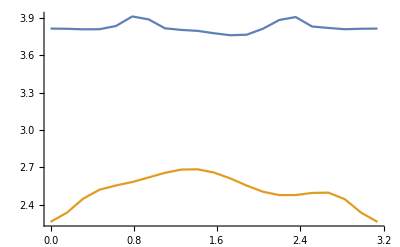

```mathematica
ListLinePlot[{tm64max,tm64mean}]
```

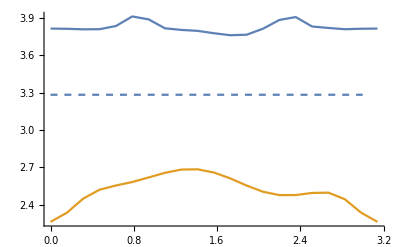

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,3},PlotStyle->Dashed],ListLinePlot[{tm64max,tm64mean}],PlotRange->All]
```

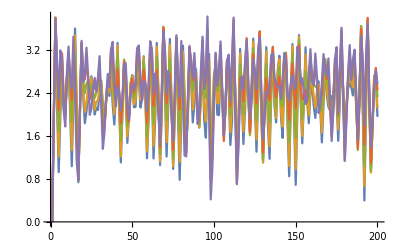

```mathematica
ListLinePlot[Table[tm64n[[n]],{n,1,5}]]
```

```mathematica
N[2*180/7]
```

51.4286

## dt = pi/4

#### data

```mathematica
tm4={-0.000000000000000000*10^+00,2.000000000000003997*10^+00,-7.688223609155823637*10^-15,2.000000000000003109*10^+00,-1.986124432365262802*10^-14,2.000000000000007550*10^+00,-1.922055902288963482*10^-14,2.000000000000011102*10^+00,-2.819015323357155213*10^-14,2.000000000000010658*10^+00,-2.370535612823058401*10^-14,2.000000000000013323*10^+00,-3.011220913586054433*10^-14,2.000000000000015543*10^+00,-3.844111804577952208*10^-14,2.000000000000015099*10^+00,-4.933276815875057358*10^-14,2.000000000000019096*10^+00,-4.484797105340954235*10^-14,2.000000000000021316*10^+00,-5.125482406103959418*10^-14,2.000000000000023981*10^+00,-5.958373297095869815*10^-14,2.000000000000023093*10^+00,-5.894304767019568918*10^-14,2.000000000000026645*10^+00,-6.791264188087785261*10^-14,2.000000000000026201*10^+00,-8.008566259537516186*10^-14,2.000000000000031086*10^+00,-7.944497729461215289*10^-14,2.000000000000034639*10^+00,-8.905525680605746413*10^-14,2.000000000000034639*10^+00,-8.521114500147933459*10^-14,2.000000000000036859*10^+00,-9.225868330987257208*10^-14,2.000000000000039524*10^+00,-1.005875922197919285*10^-13,2.000000000000039080*10^+00,-9.994690691902889428*10^-14,2.000000000000042633*10^+00,-1.089165011297113101*10^-13,2.000000000000042188*10^+00,-1.210895218442089728*10^-13,2.000000000000047073*10^+00,-1.204488365434459133*10^-13,2.000000000000050182*10^+00,-1.300591160548915023*10^-13,2.000000000000054179*10^+00,-1.383880249648110732*10^-13,2.000000000000053291*10^+00,-1.492796750777828821*10^-13,2.000000000000057732*10^+00,-1.454355632732046010*10^-13,2.000000000000060396*10^+00,-1.531237868823611883*10^-13,2.000000000000059064*10^+00,-1.486389897770198478*10^-13,2.000000000000061284*10^+00,-1.556865280854134009*10^-13,2.000000000000063949*10^+00,-1.640154369953331233*10^-13,2.000000000000063505*10^+00,-1.742664018075420494*10^-13,2.000000000000067057*10^+00,-1.697816047022006332*10^-13,2.000000000000069278*10^+00,-1.774698283113573719*10^-13,2.000000000000072387*10^+00,-1.864394225220402548*10^-13,2.000000000000071942*10^+00,-1.845173666197510512*10^-13,2.000000000000075051*10^+00,-1.922055902289078656*10^-13,2.000000000000074163*10^+00,-2.043786109434062225*10^-13,2.000000000000079048*10^+00,-2.037379256426431630*10^-13,2.000000000000082601*10^+00,-2.127075198533261973*10^-13,2.000000000000086153*10^+00,-2.203957434624831885*10^-13,2.000000000000085265*10^+00,-2.312873935754555779*10^-13,2.000000000000088818*10^+00,-2.274432817708770697*10^-13,2.000000000000091482*10^+00,-2.351315053800341366*10^-13,2.000000000000090594*10^+00,-2.306467082746924680*10^-13,2.000000000000092815*10^+00,-2.376942465830864754*10^-13,2.000000000000095923*10^+00,-2.460231554930066522*10^-13,2.000000000000095035*10^+00,-2.453824701922435927*10^-13,2.000000000000098588*10^+00,-2.537113791021638201*10^-13,2.000000000000097700*10^+00,-2.658843998166627070*10^-13,2.000000000000102585*10^+00,-2.652437145158995971*10^-13,2.000000000000106137*10^+00,-2.742133087265829848*10^-13,2.000000000000106137*10^+00,-2.697285116212413162*10^-13,2.000000000000107914*10^+00,-2.761353646288723147*10^-13,2.000000000000110578*10^+00,-2.844642735387927439*10^-13,2.000000000000109690*10^+00,-2.953559236517656634*10^-13,2.000000000000114131*10^+00,-2.908711265464238938*10^-13,2.000000000000116351*10^+00,-2.972779795540549933*10^-13,2.000000000000118572*10^+00,-3.056068884639755235*10^-13,2.000000000000118128*10^+00,-3.049662031632124136*10^-13,2.000000000000121680*10^+00,-3.139357973738961042*10^-13,2.000000000000121680*10^+00,-3.261088180883954961*10^-13,2.000000000000126121*10^+00,-3.254681327876323356*10^-13,2.000000000000129674*10^+00,-3.350784122990792877*10^-13,2.000000000000129230*10^+00,-3.312343004945004766*10^-13,2.000000000000131894*10^+00,-3.382818388028949384*10^-13,2.000000000000134559*10^+00,-3.466107477128157211*10^-13,2.000000000000134115*10^+00,-3.459700624120525606*10^-13,2.000000000000137224*10^+00,-3.549396566227365542*10^-13,2.000000000000136779*10^+00,-3.671126773372362490*10^-13,2.000000000000142109*10^+00,-3.664719920364731390*10^-13,2.000000000000145217*10^+00,-3.760822715479203435*10^-13,2.000000000000149214*10^+00,-3.844111804578413282*10^-13,2.000000000000148326*10^+00,-3.953028305708150050*10^-13,2.000000000000152767*10^+00,-3.914587187662360424*10^-13,2.000000000000154987*10^+00,-3.991469423753939676*10^-13,2.000000000000154099*10^+00,-3.946621452700517941*10^-13,2.000000000000156319*10^+00,-4.017096835784465588*10^-13,2.000000000000158984*10^+00,-4.100385924883676949*10^-13,2.000000000000158096*10^+00,-4.093979071876045849*10^-13,2.000000000000162093*10^+00,-4.177268160975257715*10^-13,2.000000000000161204*10^+00,-4.298998368120259711*10^-13,2.000000000000166089*10^+00,-4.292591515112628612*10^-13,2.000000000000169642*10^+00,-4.382287457219473092*10^-13,2.000000000000168754*10^+00,-4.337439486166050852*10^-13,2.000000000000171418*10^+00,-4.401508016242368410*10^-13,2.000000000000174083*10^+00,-4.484797105341581790*10^-13,2.000000000000173195*10^+00,-4.593713606471323607*10^-13,2.000000000000177636*10^+00,-4.548865635417899852*10^-13,2.000000000000179412*10^+00,-4.612934165494218925*10^-13,2.000000000000182077*10^+00,-4.696223254593433315*10^-13,2.000000000000181188*10^+00,-4.689816401585802215*10^-13,2.000000000000184741*10^+00,-4.779512343692648714*10^-13,2.000000000000184741*10^+00,-4.901242550837656769*10^-13,2.000000000000189626*10^+00,-4.894835697830024660*10^-13,2.000000000000192735*10^+00,-4.990938492944505288*10^-13,2.000000000000196732*10^+00,-5.074227582043721697*10^-13,2.000000000000195399*10^+00,-5.183144083173467553*10^-13,2.000000000000200284*10^+00,-5.144702965127674898*10^-13,2.000000000000202505*10^+00,2.722912528242654327*10^-14,1.929680324037560402*10^+00,1.986124432365235034*10^-14,1.929680324037559513*10^+00,8.809422885490996247*10^-15,1.929680324037563066*10^+00,1.057130746258919045*10^-14,1.929680324037566619*10^+00,1.922055902288949598*10^-15,1.929680324037566397*10^+00,4.324625780150133047*10^-15,1.929680324037569061*10^+00,-4.164454454959398948*10^-15,1.929680324037572614*10^+00,-1.249336336487823313*10^-14,1.929680324037572170*10^+00,-2.274432817708609580*10^-14,1.929680324037576167*10^+00,-2.018158697403411988*10^-14,1.929680324037578831*10^+00,-2.819015323357155213*10^-14,1.929680324037582162*10^+00,-3.523769154196452141*10^-14,1.929680324037581052*10^+00,-3.331563563967552606*10^-14,1.929680324037584160*10^+00,-4.132420189921303089*10^-14,1.929680324037583494*10^+00,-5.349722261371011295*10^-14,1.929680324037587935*10^+00,-5.221585201218410132*10^-14,1.929680324037591266*10^+00,-6.022441827172170712*10^-14,1.929680324037590378*10^+00,-5.894304767019568918*10^-14,1.929680324037594374*10^+00,-6.759229923049634813*10^-14,1.929680324037597483*10^+00,-7.624155079079705756*10^-14,1.929680324037597039*10^+00,-7.496018018927102700*10^-14,1.929680324037600148*10^+00,-8.296874644880875271*10^-14,1.929680324037599704*10^+00,-9.482142451292468369*10^-14,1.929680324037604144*10^+00,-9.289936861063560630*10^-14,1.929680324037607253*10^+00,-1.015486201709364546*10^-13,1.929680324037610806*10^+00,-1.098775290808558615*10^-13,1.929680324037610584*10^+00,-1.214098644945905025*10^-13,1.929680324037614358*10^+00,-1.194878085923013747*10^-13,1.929680324037617467*10^+00,-1.278167175022208951*10^-13,1.929680324037617023*10^+00,-1.268556895510763312*10^-13,1.929680324037620576*10^+00,-1.345439131602328175*10^-13,1.929680324037623684*10^+00,-1.422321367693893543*10^-13,1.929680324037622796*10^+00,-1.521627589312166244*10^-13,1.929680324037626571*10^+00,-1.499203603785459415*10^-13,1.929680324037629680*10^+00,-1.572882413373210243*10^-13,1.929680324037632788*10^+00,-1.656171502472407467*10^-13,1.929680324037632344*10^+00,-1.636950943449515936*10^-13,1.929680324037635231*10^+00,-1.717036606044898116*10^-13,1.929680324037634565*10^+00,-1.829156533678434025*10^-13,1.929680324037638783*10^+00,-1.813139401159357539*10^-13,1.929680324037642114*10^+00,-1.886818210747110134*10^-13,1.929680324037644779*10^+00,-1.963700446838678278*10^-13,1.929680324037644557*10^+00,-2.075820374472215955*10^-13,1.929680324037648109*10^+00,-2.063006668456954513*10^-13,1.929680324037651662*10^+00,-2.130278625037077523*10^-13,1.929680324037650774*10^+00,-2.104651213006554388*10^-13,1.929680324037653882*10^+00,-2.191143728609569938*10^-13,1.929680324037656991*10^+00,-2.268025964701139850*10^-13,1.929680324037656547*10^+00,-2.255212258685878408*10^-13,1.929680324037659656*10^+00,-2.322484215266002428*10^-13,1.929680324037658323*10^+00,-2.428197289891911530*10^-13,1.929680324037662320*10^+00,-2.402569877861388142*10^-13,1.929680324037664985*10^+00,-2.473045260945328721*10^-13,1.929680324037664096*10^+00,-2.453824701922435927*10^-13,1.929680324037666983*10^+00,-2.533910364517822651*10^-13,1.929680324037670758*10^+00,-2.610792600609394329*10^-13,1.929680324037669870*10^+00,-2.722912528242937055*10^-13,1.929680324037674088*10^+00,-2.697285116212413162*10^-13,1.929680324037676753*10^+00,-2.770963925800169796*10^-13,1.929680324037679640*10^+00,-2.857456441403189638*10^-13,1.929680324037679195*10^+00,-2.841439308884111385*10^-13,1.929680324037682304*10^+00,-2.918321544975685083*10^-13,1.929680324037681860*10^+00,-3.027238046105414783*10^-13,1.929680324037685857*10^+00,-3.004814060578705935*10^-13,1.929680324037688743*10^+00,-3.081696296670280138*10^-13,1.929680324037688077*10^+00,-3.056068884639755235*10^-13,1.929680324037690964*10^+00,-3.136154547235144988*10^-13,1.929680324037694072*10^+00,-3.219443636334351300*10^-13,1.929680324037693628*10^+00,-3.203426503815273551*10^-13,1.929680324037696959*10^+00,-3.289919019418295413*10^-13,1.929680324037696515*10^+00,-3.402038947051843692*10^-13,1.929680324037700956*10^+00,-3.382818388028949384*10^-13,1.929680324037703620*10^+00,-3.456497197616710057*10^-13,1.929680324037706507*10^+00,-3.539786286715918388*10^-13,1.929680324037706285*10^+00,-3.635889081830389928*10^-13,1.929680324037709838*10^+00,-3.626278802318942269*10^-13,1.929680324037712946*10^+00,-3.696754185402888402*10^-13,1.929680324037712280*10^+00,-3.677533626379994094*10^-13,1.929680324037715611*10^+00,-3.748009009463940732*10^-13,1.929680324037718275*10^+00,-3.821687819051702919*10^-13,1.929680324037716943*10^+00,-3.805670686532624161*10^-13,1.929680324037720496*10^+00,-3.892163202135650061*10^-13,1.929680324037720052*10^+00,-4.007486556273018434*10^-13,1.929680324037724048*10^+00,-3.988265997250124126*10^-13,1.929680324037727601*10^+00,-4.061944806837887323*10^-13,1.929680324037726713*10^+00,-4.042724247814992510*10^-13,1.929680324037729822*10^+00,-4.126013336914203871*10^-13,1.929680324037732930*10^+00,-4.209302426013416242*10^-13,1.929680324037732486*10^+00,-4.321422353646971084*10^-13,1.929680324037736705*10^+00,-4.295794941616444162*10^-13,1.929680324037739592*10^+00,-4.369473751204209378*10^-13,1.929680324037742700*10^+00,-4.452762840303422759*10^-13,1.929680324037741812*10^+00,-4.433542281280527441*10^-13,1.929680324037744921*10^+00,-4.516831370379740821*10^-13,1.929680324037744477*10^+00,-4.628951298013298693*10^-13,1.929680324037748473*10^+00,-4.616137591998035484*10^-13,1.929680324037752026*10^+00,-4.696223254593433315*10^-13,1.929680324037755357*10^+00,-4.776308917188833165*10^-13,1.929680324037754469*10^+00,-4.894835697830024660*10^-13,1.929680324037759132*10^+00,-4.872411712303312783*10^-13,1.929680324037761796*10^+00,-9.610279511444755881*10^-16,1.729030204872848975*10^+00,-6.086510357248356435*10^-15,1.729030204872848087*10^+00,-1.537644721831168830*10^-14,1.729030204872851417*10^+00,-1.345439131602271819*10^-14,1.729030204872854526*10^+00,-1.986124432365262802*10^-14,1.729030204872853860*10^+00,-1.825953107174514661*10^-14,1.729030204872856746*10^+00,-2.434604142899358036*10^-14,1.729030204872859855*10^+00,-3.107323708700503885*10^-14,1.729030204872859411*10^+00,-4.100385924883153271*10^-14,1.729030204872862964*10^+00,-3.876146069616102657*10^-14,1.729030204872865850*10^+00,-4.484797105340954235*10^-14,1.729030204872868737*10^+00,-5.093448141065808969*10^-14,1.729030204872868071*10^+00,-4.933276815875057358*10^-14,1.729030204872871401*10^+00,-5.638030646714365331*10^-14,1.729030204872870957*10^+00,-6.631092862897031757*10^-14,1.729030204872874066*10^+00,-6.406853007629977355*10^-14,1.729030204872877174*10^+00,-7.175675368545594429*10^-14,1.729030204872877396*10^+00,-7.047538308392991373*10^-14,1.729030204872880727*10^+00,-7.656189344117856204*10^-14,1.729030204872883170*10^+00,-8.264840379842724822*10^-14,1.729030204872882726*10^+00,-8.072634789613818345*10^-14,1.729030204872885390*10^+00,-8.713320090376839936*10^-14,1.729030204872885168*10^+00,-9.642313776483224398*10^-14,1.729030204872888277*10^+00,-9.482142451292468369*10^-14,1.729030204872891385*10^+00,-1.005875922197919285*10^-13,1.729030204872894272*10^+00,-1.066741025770407030*10^-13,1.729030204872893606*10^+00,-1.172454100396307423*10^-13,1.729030204872897158*10^+00,-1.159640394381046739*10^-13,1.729030204872900711*10^+00,-1.226912350961165457*10^-13,1.729030204872900045*10^+00,-1.210895218442089728*10^-13,1.729030204872903376*10^+00,-1.268556895510763312*10^-13,1.729030204872906040*10^+00,-1.335828852090882535*10^-13,1.729030204872906040*10^+00,-1.422321367693893543*10^-13,1.729030204872908927*10^+00,-1.403100808671002264*10^-13,1.729030204872911813*10^+00,-1.463965912243491650*10^-13,1.729030204872914478*10^+00,-1.528034442319796586*10^-13,1.729030204872914034*10^+00,-1.524831015815981288*10^-13,1.729030204872917587*10^+00,-1.585696119388471179*10^-13,1.729030204872917365*10^+00,-1.688205767510560440*10^-13,1.729030204872920695*10^+00,-1.665781781983853359*10^-13,1.729030204872923138*10^+00,-1.726646885556344007*10^-13,1.729030204872926690*10^+00,-1.777901709617388764*10^-13,1.729030204872925580*10^+00,-1.877207931235663989*10^-13,1.729030204872929133*10^+00,-1.854783945708956656*10^-13,1.729030204872931797*10^+00,-1.915649049281448061*10^-13,1.729030204872930909*10^+00,-1.902835343266186620*10^-13,1.729030204872934018*10^+00,-1.966903873342493575*10^-13,1.729030204872937126*10^+00,-2.037379256426431630*10^-13,1.729030204872936682*10^+00,-2.021362123907354639*10^-13,1.729030204872939791*10^+00,-2.082227227479846802*10^-13,1.729030204872939347*10^+00,-2.175126596090492947*10^-13,1.729030204872942234*10^+00,-2.146295757556154514*10^-13,1.729030204872945120*10^+00,-2.210364287632462732*10^-13,1.729030204872944454*10^+00,-2.194347155113385488*10^-13,1.729030204872947341*10^+00,-2.255212258685878408*10^-13,1.729030204872950449*10^+00,-2.325687641769817978*10^-13,1.729030204872950005*10^+00,-2.421790436884280935*10^-13,1.729030204872953558*10^+00,-2.399366451357572592*10^-13,1.729030204872956666*10^+00,-2.460231554930066522*10^-13,1.729030204872959553*10^+00,-2.533910364517822651*10^-13,1.729030204872959109*10^+00,-2.508282952487298758*10^-13,1.729030204872962218*10^+00,-2.562741203052162093*10^-13,1.729030204872961329*10^+00,-2.658843998166627070*10^-13,1.729030204872964660*10^+00,-2.649233718655180421*10^-13,1.729030204872967547*10^+00,-2.713302248731490406*10^-13,1.729030204872967325*10^+00,-2.697285116212413162*10^-13,1.729030204872970877*10^+00,-2.761353646288723147*10^-13,1.729030204872973098*10^+00,-2.825422176365034141*10^-13,1.729030204872972876*10^+00,-2.812608470349771942*10^-13,1.729030204872976206*10^+00,-2.883083853433714036*10^-13,1.729030204872975984*10^+00,-2.969576369036734383*10^-13,1.729030204872979315*10^+00,-2.956762663021471679*10^-13,1.729030204872982202*10^+00,-3.017627766593968134*10^-13,1.729030204872985088*10^+00,-3.078492870166464083*10^-13,1.729030204872984200*10^+00,-3.164985385769485945*10^-13,1.729030204872987309*10^+00,-3.145764826746592142*10^-13,1.729030204872990417*10^+00,-3.209833356822904651*10^-13,1.729030204872989973*10^+00,-3.190612797800010847*10^-13,1.729030204872992860*10^+00,-3.245071048364876707*10^-13,1.729030204872995524*10^+00,-3.299529298929742567*10^-13,1.729030204872994636*10^+00,-3.280308739906848259*10^-13,1.729030204872997967*10^+00,-3.350784122990792877*10^-13,1.729030204872997523*10^+00,-3.450090344609078957*10^-13,1.729030204873001075*10^+00,-3.450090344609078957*10^-13,1.729030204873004628*10^+00,-3.520565727693024080*10^-13,1.729030204873004850*10^+00,-3.507752021677761376*10^-13,1.729030204873007515*10^+00,-3.571820551754075400*10^-13,1.729030204873010845*10^+00,-3.632685655326574379*10^-13,1.729030204873010179*10^+00,-3.725585023937230369*10^-13,1.729030204873013510*10^+00,-3.706364464914336061*10^-13,1.729030204873016618*10^+00,-3.773636421494466644*10^-13,1.729030204873019283*10^+00,-3.821687819051702919*10^-13,1.729030204873018617*10^+00,-3.796060407021176502*10^-13,1.729030204873021059*10^+00,-3.850518657586044886*10^-13,1.729030204873020393*10^+00,-3.940214599692886336*10^-13,1.729030204873023724*10^+00,-3.927400893677623633*10^-13,1.729030204873026833*10^+00,-3.988265997250124126*10^-13,1.729030204873029719*10^+00,-4.049131100822624114*10^-13,1.729030204873029053*10^+00,-4.138827042929467584*10^-13,1.729030204873032162*10^+00,-4.116403057402756212*10^-13,1.729030204873035270*10^+00,9.610279511444749964*10^-16,1.427593131110277636*10^+00,-2.562741203051936479*10^-15,1.427593131110277413*10^+00,-8.969594210681797399*10^-15,1.427593131110280078*10^+00,-6.406853007629849876*10^-15,1.427593131110282965*10^+00,-1.057130746258926618*10^-14,1.427593131110282521*10^+00,-9.930622161826277720*10^-15,1.427593131110286073*10^+00,-1.377473396640421163*10^-14,1.427593131110289404*10^+00,-1.793918842136365160*10^-14,1.427593131110288738*10^+00,-2.498672672975657355*10^-14,1.427593131110292290*10^+00,-2.434604142899358036*10^-14,1.427593131110294733*10^+00,-2.819015323357155213*10^-14,1.427593131110298508*10^+00,-3.107323708700503885*10^-14,1.427593131110298730*10^+00,-2.947152383509754167*10^-14,1.427593131110301838*10^+00,-3.299529298929403420*10^-14,1.427593131110301172*10^+00,-3.908180334654252474*10^-14,1.427593131110303837*10^+00,-3.780043274501652574*10^-14,1.427593131110306945*10^+00,-4.100385924883153271*10^-14,1.427593131110306723*10^+00,-3.940214599692402922*10^-14,1.427593131110309166*10^+00,-4.260557250073902989*10^-14,1.427593131110312719*10^+00,-4.548865635417254501*10^-14,1.427593131110312052*10^+00,-4.388694310226504152*10^-14,1.427593131110315383*10^+00,-4.741071225646155929*10^-14,1.427593131110314939*10^+00,-5.413790791447312823*10^-14,1.427593131110317826*10^+00,-5.253619466256560580*10^-14,1.427593131110320268*10^+00,-5.541927851599913985*10^-14,1.427593131110323155*10^+00,-5.862270501981418470*10^-14,1.427593131110322489*10^+00,-6.534990067782580411*10^-14,1.427593131110325597*10^+00,-6.438887272668129066*10^-14,1.427593131110328706*10^+00,-6.759229923049634813*10^-14,1.427593131110328040*10^+00,-6.567024332820730860*10^-14,1.427593131110330926*10^+00,-6.919401248240388317*10^-14,1.427593131110334479*10^+00,-7.303812428698197485*10^-14,1.427593131110334479*10^+00,-8.040600524575667897*10^-14,1.427593131110336921*10^+00,-7.912463464423063579*10^-14,1.427593131110341140*10^+00,-8.296874644880875271*10^-14,1.427593131110343805*10^+00,-8.681285825338688225*10^-14,1.427593131110343583*10^+00,-8.457045970071631300*10^-14,1.427593131110346025*10^+00,-8.745354355414990384*10^-14,1.427593131110345803*10^+00,-9.418073921216164948*10^-14,1.427593131110348024*10^+00,-9.225868330987257208*10^-14,1.427593131110351132*10^+00,-9.610279511445072687*10^-14,1.427593131110354019*10^+00,-9.994690691902889428*10^-14,1.427593131110354241*10^+00,-1.060334172762776688*10^-13,1.427593131110356683*10^+00,-1.044317040243700959*10^-13,1.427593131110360014*10^+00,-1.076351305281852417*10^-13,1.427593131110359348*10^+00,-1.063537599266591859*10^-13,1.427593131110362235*10^+00,-1.101978717312373786*10^-13,1.427593131110365787*10^+00,-1.134012982350525370*10^-13,1.427593131110366009*10^+00,-1.121199276335264686*10^-13,1.427593131110368452*10^+00,-1.153233541373416396*10^-13,1.427593131110368230*10^+00,-1.226912350961165457*10^-13,1.427593131110371338*10^+00,-1.214098644945905025*10^-13,1.427593131110374225*10^+00,-1.252539762991687331*10^-13,1.427593131110373781*10^+00,-1.226912350961165457*10^-13,1.427593131110377112*10^+00,-1.262150042503132717*10^-13,1.427593131110379998*10^+00,-1.303794587052730572*10^-13,1.427593131110379332*10^+00,-1.371066543632849796*10^-13,1.427593131110382441*10^+00,-1.355049411113773814*10^-13,1.427593131110385771*10^+00,-1.393490529159556372*10^-13,1.427593131110389102*10^+00,-1.435135073709154732*10^-13,1.427593131110388880*10^+00,-1.425524794197708840*10^-13,1.427593131110392211*10^+00,-1.451152206228230713*10^-13,1.427593131110391544*10^+00,-1.528034442319796586*10^-13,1.427593131110394431*10^+00,-1.515220736304535649*10^-13,1.427593131110397540*10^+00,-1.550458427846503414*10^-13,1.427593131110397096*10^+00,-1.528034442319796586*10^-13,1.427593131110400204*10^+00,-1.560068707357949306*10^-13,1.427593131110403313*10^+00,-1.608120104915178260*10^-13,1.427593131110403313*10^+00,-1.598509825403732621*10^-13,1.427593131110406866*10^+00,-1.627340663938070044*10^-13,1.427593131110406643*10^+00,-1.697816047022006332*10^-13,1.427593131110409086*10^+00,-1.694612620518191035*10^-13,1.427593131110412861*10^+00,-1.723443459052528710*10^-13,1.427593131110415747*10^+00,-1.755477724090681683*10^-13,1.427593131110415303*10^+00,-1.819546254166987881*10^-13,1.427593131110417302*10^+00,-1.800325695144096097*10^-13,1.427593131110420188*10^+00,-1.841970239693695467*10^-13,1.427593131110420188*10^+00,-1.825953107174618475*10^-13,1.427593131110422853*10^+00,-1.867597651724217845*10^-13,1.427593131110426405*10^+00,-1.906038769770002170*10^-13,1.427593131110425961*10^+00,-1.893225063754740476*10^-13,1.427593131110429292*10^+00,-1.922055902289078656*10^-13,1.427593131110428404*10^+00,-1.982921005861570314*10^-13,1.427593131110430846*10^+00,-1.966903873342493575*10^-13,1.427593131110433289*10^+00,-1.998938138380647053*10^-13,1.427593131110433511*10^+00,-1.986124432365385611*10^-13,1.427593131110437064*10^+00,-2.018158697403539089*10^-13,1.427593131110439728*10^+00,-2.053396388945508369*10^-13,1.427593131110439284*10^+00,-2.123871772029446929*10^-13,1.427593131110442393*10^+00,-2.111058066014185235*10^-13,1.427593131110445057*10^+00,-2.146295757556154514*10^-13,1.427593131110448610*10^+00,-2.184736875601939344*10^-13,1.427593131110448166*10^+00,-2.175126596090492947*10^-13,1.427593131110451496*10^+00,-2.203957434624831885*10^-13,1.427593131110451274*10^+00,-2.261619111693509003*10^-13,1.427593131110453939*10^+00,-2.252008832182063111*10^-13,1.427593131110456603*10^+00,-2.287246523724032391*10^-13,1.427593131110459934*10^+00,-2.325687641769817978*10^-13,1.427593131110459712*10^+00,-2.383349318838495853*10^-13,1.427593131110461488*10^+00,-2.364128759815602555*10^-13,1.427593131110464597*10^+00,4.805139755722374982*10^-16,1.070009614893125738*10^+00,9.610279511444749964*10^-16,1.070009614893125960*10^+00,-1.601713251907459708*10^-15,1.070009614893127958*10^+00,-0.000000000000000000*10^+00,1.070009614893132399*10^+00,-0.000000000000000000*10^+00,1.070009614893132399*10^+00,1.281370601525966465*10^-15,1.070009614893136174*10^+00,1.441541926716712396*10^-15,1.070009614893139949*10^+00,1.601713251907457933*10^-15,1.070009614893140171*10^+00,-1.281370601525967648*10^-15,1.070009614893142391*10^+00,-3.203426503814917641*10^-16,1.070009614893145944*10^+00,-0.000000000000000000*10^+00,1.070009614893150607*10^+00,-0.000000000000000000*10^+00,1.070009614893150385*10^+00,1.121199276335220928*10^-15,1.070009614893154826*10^+00,9.610279511444749964*10^-16,1.070009614893154604*10^+00,-2.242398552670444222*10^-15,1.070009614893157046*10^+00,-1.601713251907459708*10^-15,1.070009614893161043*10^+00,-2.242398552670444222*10^-15,1.070009614893161487*10^+00,-9.610279511444755881*10^-16,1.070009614893164818*10^+00,-1.601713251907459708*10^-15,1.070009614893168592*10^+00,-1.922055902288951571*10^-15,1.070009614893169037*10^+00,-1.281370601525967648*10^-15,1.070009614893173033*10^+00,-1.281370601525967648*10^-15,1.070009614893173255*10^+00,-4.805139755722384251*10^-15,1.070009614893175476*10^+00,-3.203426503814921388*10^-15,1.070009614893179029*10^+00,-3.844111804577906297*10^-15,1.070009614893183469*10^+00,-3.844111804577906297*10^-15,1.070009614893183247*10^+00,-7.367880958774330197*10^-15,1.070009614893185912*10^+00,-6.086510357248356435*10^-15,1.070009614893189909*10^+00,-6.406853007629849876*10^-15,1.070009614893190131*10^+00,-5.125482406103877692*10^-15,1.070009614893193906*10^+00,-5.445825056485370343*10^-15,1.070009614893198124*10^+00,-4.484797105340891600*10^-15,1.070009614893197458*10^+00,-7.047538308392836756*10^-15,1.070009614893199679*10^+00,-5.766167706866862995*10^-15,1.070009614893203675*10^+00,-5.766167706866862995*10^-15,1.070009614893207672*10^+00,-6.086510357248356435*10^-15,1.070009614893208116*10^+00,-5.125482406103877692*10^-15,1.070009614893212113*10^+00,-4.805139755722384251*10^-15,1.070009614893212113*10^+00,-8.328908909918808940*10^-15,1.070009614893214778*10^+00,-6.727195658011343316*10^-15,1.070009614893218330*10^+00,-7.047538308392836756*10^-15,1.070009614893222771*10^+00,-7.367880958774330197*10^-15,1.070009614893222549*10^+00,-1.025096481220777274*10^-14,1.070009614893224326*10^+00,-8.649251560300303958*10^-15,1.070009614893228322*10^+00,-8.328908909918808940*10^-15,1.070009614893228989*10^+00,-7.047538308392836756*10^-15,1.070009614893232985*10^+00,-7.367880958774330197*10^-15,1.070009614893236316*10^+00,-7.367880958774330197*10^-15,1.070009614893236760*10^+00,-5.766167706866862995*10^-15,1.070009614893240091*10^+00,-5.766167706866862995*10^-15,1.070009614893240313*10^+00,-9.289936861063290839*10^-15,1.070009614893242755*10^+00,-8.328908909918808940*10^-15,1.070009614893246974*10^+00,-7.688223609155823637*10^-15,1.070009614893247196*10^+00,-6.406853007629849876*10^-15,1.070009614893250749*10^+00,-6.406853007629849876*10^-15,1.070009614893254746*10^+00,-6.406853007629849876*10^-15,1.070009614893254302*10^+00,-1.025096481220777274*10^-14,1.070009614893256966*10^+00,-8.649251560300303958*10^-15,1.070009614893260963*10^+00,-9.289936861063290839*10^-15,1.070009614893264738*10^+00,-9.930622161826277720*10^-15,1.070009614893264960*10^+00,-8.328908909918808940*10^-15,1.070009614893269179*10^+00,-8.649251560300303958*10^-15,1.070009614893269179*10^+00,-1.153233541373374966*10^-14,1.070009614893271399*10^+00,-9.930622161826277720*10^-15,1.070009614893275174*10^+00,-9.610279511444785857*10^-15,1.070009614893275174*10^+00,-8.328908909918808940*10^-15,1.070009614893279171*10^+00,-8.328908909918808940*10^-15,1.070009614893283167*10^+00,-8.969594210681797399*10^-15,1.070009614893283389*10^+00,-7.688223609155823637*10^-15,1.070009614893287164*10^+00,-7.688223609155823637*10^-15,1.070009614893287830*10^+00,-1.121199276335225464*10^-14,1.070009614893290051*10^+00,-9.610279511444785857*10^-15,1.070009614893293381*10^+00,-9.610279511444785857*10^-15,1.070009614893297156*10^+00,-1.025096481220777274*10^-14,1.070009614893297600*10^+00,-1.409507661678570664*10^-14,1.070009614893300043*10^+00,-1.281370601525972815*10^-14,1.070009614893304040*10^+00,-1.281370601525972815*10^-14,1.070009614893304262*10^+00,-1.185267806411524467*10^-14,1.070009614893308036*10^+00,-1.217302071449673811*10^-14,1.070009614893311145*10^+00,-1.217302071449673811*10^-14,1.070009614893312033*10^+00,-1.153233541373374966*10^-14,1.070009614893315586*10^+00,-1.217302071449673811*10^-14,1.070009614893316030*10^+00,-1.505610456793019328*10^-14,1.070009614893318028*10^+00,-1.345439131602271819*10^-14,1.070009614893322025*10^+00,-1.345439131602271819*10^-14,1.070009614893322469*10^+00,-1.313404866564122317*10^-14,1.070009614893326688*10^+00,-1.345439131602271819*10^-14,1.070009614893330241*10^+00,-1.345439131602271819*10^-14,1.070009614893330019*10^+00,-1.697816047021916339*10^-14,1.070009614893332905*10^+00,-1.601713251907467518*10^-14,1.070009614893337124*10^+00,-1.601713251907467518*10^-14,1.070009614893340899*10^+00,-1.601713251907467518*10^-14,1.070009614893340899*10^+00,-1.409507661678570664*10^-14,1.070009614893344452*10^+00,-1.505610456793019328*10^-14,1.070009614893344452*10^+00,-1.793918842136365160*10^-14,1.070009614893346894*10^+00,-1.697816047021916339*10^-14,1.070009614893350669*10^+00,-1.633747516945617335*10^-14,1.070009614893354444*10^+00,-1.665781781983766837*10^-14,1.070009614893354666*10^+00,-1.954090167327112984*10^-14,1.070009614893357330*10^+00,-1.793918842136365160*10^-14,1.070009614893361327*10^+00,3.203426503814917641*10^-16,7.091578053305441776*10^-01,3.844111804577896041*10^-15,7.091578053305457319*10^-01,4.324625780150133047*10^-15,7.091578053305480633*10^-01,6.246681682439076334*10^-15,7.091578053305537255*10^-01,1.025096481220770016*10^-14,7.091578053305541696*10^-01,1.137216408854291222*10^-14,7.091578053305598317*10^-01,1.521627589312077828*10^-14,7.091578053305649387*10^-01,1.857987372212640182*10^-14,7.091578053305658269*10^-01,1.938073034808011885*10^-14,7.091578053305684914*10^-01,2.066210094960607053*10^-14,7.091578053305747087*10^-01,2.418587010380242737*10^-14,7.091578053305802598*10^-01,2.770963925799877160*10^-14,7.091578053305810370*10^-01,2.931135250990620251*10^-14,7.091578053305864771*10^-01,3.267495033891179134*10^-14,7.091578053305874763*10^-01,3.299529298929327058*10^-14,7.091578053305904739*10^-01,3.411649226562846686*10^-14,7.091578053305960250*10^-01,3.731991876944330975*10^-14,7.091578053305963580*10^-01,3.844111804577849972*10^-14,7.091578053306015761*10^-01,4.260557250073778034*10^-14,7.091578053306077933*10^-01,4.677002695569704202*10^-14,7.091578053306082374*10^-01,4.789122623203222568*10^-14,7.091578053306136775*10^-01,5.125482406103777033*10^-14,7.091578053306146767*10^-01,5.189550936180072881*10^-14,7.091578053306173413*10^-01,5.349722261370813764*10^-14,7.091578053306233365*10^-01,5.702099176790440298*10^-14,7.091578053306292206*10^-01,6.070493224729141425*10^-14,7.091578053306296647*10^-01,6.086510357248215387*10^-14,7.091578053306318852*10^-01,6.214647417400807083*10^-14,7.091578053306385465*10^-01,6.599058597858579648*10^-14,7.091578053306388796*10^-01,6.743212790530244044*10^-14,7.091578053306445417*10^-01,7.175675368545237233*10^-14,7.091578053306499818*10^-01,7.496018018926712687*10^-14,7.091578053306506479*10^-01,7.560086549003007273*10^-14,7.091578053306535345*10^-01,7.752292139231892293*10^-14,7.091578053306587526*10^-01,8.104669054651513147*10^-14,7.091578053306648588*10^-01,8.505097367628355888*10^-14,7.091578053306650808*10^-01,8.633234427780945060*10^-14,7.091578053306708540*10^-01,8.969594210681490690*10^-14,7.091578053306717422*10^-01,9.017645608238711314*10^-14,7.091578053306742957*10^-01,9.129765535872226524*10^-14,7.091578053306799578*10^-01,9.466125318772770891*10^-14,7.091578053306851759*10^-01,9.786467969154241297*10^-14,7.091578053306863971*10^-01,9.866553631749608583*10^-14,7.091578053306890617*10^-01,1.001070782442127045*10^-13,7.091578053306945018*10^-01,1.039511900487903418*10^-13,7.091578053306949458*10^-01,1.057130746258884019*10^-13,7.091578053307002749*10^-01,1.092368437800845600*10^-13,7.091578053307067142*10^-01,1.130809555846621594*10^-13,7.091578053307074914*10^-01,1.146826688365694925*10^-13,7.091578053307130425*10^-01,1.182064379907656127*10^-13,7.091578053307137086*10^-01,1.185267806411470667*10^-13,7.091578053307169283*10^-01,1.194878085922914792*10^-13,7.091578053307220353*10^-01,1.230115777464875994*10^-13,7.091578053307231455*10^-01,1.244531196732041928*10^-13,7.091578053307283636*10^-01,1.279768888274002878*10^-13,7.091578053307343588*10^-01,1.319811719571685890*10^-13,7.091578053307349139*10^-01,1.324616859327407700*10^-13,7.091578053307382445*10^-01,1.343837418350295444*10^-13,7.091578053307436846*10^-01,1.377473396640348871*10^-13,7.091578053307494578*10^-01,1.415914514686124361*10^-13,7.091578053307499019*10^-01,1.430329933953289791*10^-13,7.091578053307560081*10^-01,1.467169338747157758*10^-13,7.091578053307567853*10^-01,1.473576191754786838*10^-13,7.091578053307593388*10^-01,1.486389897770045250*10^-13,7.091578053307658891*10^-01,1.528034442319634775*10^-13,7.091578053307662222*10^-01,1.540848148334893187*10^-13,7.091578053307711071*10^-01,1.577687553128760901*10^-13,7.091578053307769913*10^-01,1.611323531418813571*10^-13,7.091578053307778795*10^-01,1.627340663937886523*10^-13,7.091578053307834306*10^-01,1.665781781983661003*10^-13,7.091578053307839857*10^-01,1.670586921739382813*10^-13,7.091578053307873164*10^-01,1.685002341006548243*10^-13,7.091578053307927565*10^-01,1.726646885556137263*10^-13,7.091578053307980856*10^-01,1.766689716853819012*10^-13,7.091578053307986407*10^-01,1.769893143357633552*10^-13,7.091578053308018603*10^-01,1.785910275876706000*10^-13,7.091578053308076335*10^-01,1.822749680670573209*10^-13,7.091578053308082996*10^-01,1.835563386685831117*10^-13,7.091578053308138507*10^-01,1.869199364975883534*10^-13,7.091578053308197349*10^-01,1.907640483021657509*10^-13,7.091578053308206231*10^-01,1.918852475785008146*10^-13,7.091578053308261742*10^-01,1.954090167326967581*10^-13,7.091578053308267293*10^-01,1.960497020334596409*10^-13,7.091578053308296159*10^-01,1.973310726349854316*10^-13,7.091578053308349450*10^-01,2.008548417891813499*10^-13,7.091578053308360552*10^-01,2.026167263662793216*10^-13,7.091578053308416063*10^-01,2.059803241952845129*10^-13,7.091578053308469354*10^-01,2.098244359998618598*10^-13,7.091578053308471574*10^-01,2.103049499754340408*10^-13,7.091578053308507101*10^-01,2.115863205769598063*10^-13,7.091578053308562613*10^-01,2.151100897311556741*10^-13,7.091578053308621454*10^-01,2.191143728609237481*10^-13,7.091578053308630336*10^-01,2.203957434624494884*10^-13,7.091578053308689178*10^-01,2.239195126166453561*10^-13,7.091578053308691398*10^-01,2.245601979174082389*10^-13,7.091578053308724705*10^-01,2.261619111693154836*10^-13,7.091578053308782437*10^-01,2.296856803235113514*10^-13,7.091578053308832397*10^-01,2.335297921280885974*10^-13,7.091578053308844609*10^-01,2.343306487540421819*10^-13,7.091578053308870144*10^-01,2.359323620059494014*10^-13,7.091578053308926766*10^-01,-9.610279511444755881*10^-16,3.871470010700694964*10^-01,5.605996381676094975*10^-15,3.871470010700713837*10^-01,9.930622161826211456*10^-15,3.871470010700747144*10^-01,1.137216408854291222*10^-14,3.871470010700811537*10^-01,1.825953107174491627*10^-14,3.871470010700827080*10^-01,2.002141564884309627*10^-14,3.871470010700892583*10^-01,2.722912528242654327*10^-14,3.871470010700961417*10^-01,3.411649226562846686*10^-14,3.871470010700978626*10^-01,3.844111804577849972*10^-14,3.871470010701011377*10^-01,3.988265997249516892*10^-14,3.871470010701072995*10^-01,4.709036960607852126*10^-14,3.871470010701141273*10^-01,5.381756526408961688*10^-14,3.871470010701157927*10^-01,5.557944984118775270*10^-14,3.871470010701220099*10^-01,6.246681682438955007*10^-14,3.871470010701242304*10^-01,6.663127127934874234*10^-14,3.871470010701280051*10^-01,6.823298453125612592*10^-14,3.871470010701342224*10^-01,7.528052283964860611*10^-14,3.871470010701354436*10^-01,7.752292139231892293*10^-14,3.871470010701425490*10^-01,8.457045970071134002*10^-14,3.871470010701490994*10^-01,9.129765535872226524*10^-14,3.871470010701503206*10^-01,9.321971126101109019*10^-14,3.871470010701570930*10^-01,1.004274208945941712*10^-13,3.871470010701582032*10^-01,1.044317040243625355*10^-13,3.871470010701620890*10^-01,1.060334172762698812*10^-13,3.871470010701689723*10^-01,1.130809555846621594*10^-13,3.871470010701751896*10^-01,1.199683225678636854*10^-13,3.871470010701771325*10^-01,1.239726056976319866*10^-13,3.871470010701794084*10^-01,1.254141476243485801*10^-13,3.871470010701864028*10^-01,1.326218572579314970*10^-13,3.871470010701881237*10^-01,1.340633991846480652*10^-13,3.871470010701948405*10^-01,1.411109374930402046*10^-13,3.871470010702010023*10^-01,1.479983044762416170*10^-13,3.871470010702025011*10^-01,1.528034442319634775*10^-13,3.871470010702063869*10^-01,1.540848148334893187*10^-13,3.871470010702128817*10^-01,1.612925244670721094*10^-13,3.871470010702189324*10^-01,1.681798914502733703*10^-13,3.871470010702210418*10^-01,1.701019473525621195*10^-13,3.871470010702274811*10^-01,1.771494856609540570*10^-13,3.871470010702296460*10^-01,1.814741114411036860*10^-13,3.871470010702329212*10^-01,1.832359960182016577*10^-13,3.871470010702393605*10^-01,1.899631916762121159*10^-13,3.871470010702451892*10^-01,1.973310726349854316*10^-13,3.871470010702474651*10^-01,2.011751844395628039*10^-13,3.871470010702506848*10^-01,2.027768976914700486*10^-13,3.871470010702569575*10^-01,2.096642646746711328*10^-13,3.871470010702582343*10^-01,2.117464919021505333*10^-13,3.871470010702648956*10^-01,2.187940302105422941*10^-13,3.871470010702702247*10^-01,2.255212258685525756*10^-13,3.871470010702721121*10^-01,2.277636244212226779*10^-13,3.871470010702783848*10^-01,2.341704774288514549*10^-13,3.871470010702796616*10^-01,2.383349318838102054*10^-13,3.871470010702831033*10^-01,2.399366451357174249*10^-13,3.871470010702904863*10^-01,2.466638407937276054*10^-13,3.871470010702913189*10^-01,2.485858966960162284*10^-13,3.871470010702973696*10^-01,2.559537776547892160*10^-13,3.871470010703044751*10^-01,2.626809733127993460*10^-13,3.871470010703058073*10^-01,2.668454277677579451*10^-13,3.871470010703100817*10^-01,2.682869696944744376*10^-13,3.871470010703165765*10^-01,2.751743366776751432*10^-13,3.871470010703227382*10^-01,2.822218749860666262*10^-13,3.871470010703246256*10^-01,2.836634169127830682*10^-13,3.871470010703306763*10^-01,2.907109552211745008*10^-13,3.871470010703324527*10^-01,2.943948957005608684*10^-13,3.871470010703351727*10^-01,2.963169516028494914*10^-13,3.871470010703420561*10^-01,3.027238046104779655*10^-13,3.871470010703432219*10^-01,3.049662031631479415*10^-13,3.871470010703493281*10^-01,3.118535701463485461*10^-13,3.871470010703562115*10^-01,3.189011084547398273*10^-13,3.871470010703573217*10^-01,3.205028217066469458*10^-13,3.871470010703649267*10^-01,3.273901886898473989*10^-13,3.871470010703657594*10^-01,3.312343004944244935*10^-13,3.871470010703685904*10^-01,3.331563563967129651*10^-13,3.871470010703756959*10^-01,3.398835520547227417*10^-13,3.871470010703824682*10^-01,3.469310903631138714*10^-13,3.871470010703836340*10^-01,3.510955448180722684*10^-13,3.871470010703868536*10^-01,3.523769154195978825*10^-13,3.871470010703935705*10^-01,3.599049677035611427*10^-13,3.871470010703953468*10^-01,3.611863383050867567*10^-13,3.871470010704013420*10^-01,3.683940479386685124*10^-13,3.871470010704077813*10^-01,3.751212435966780871*10^-13,3.871470010704095577*10^-01,3.767229568485851551*10^-13,3.871470010704156084*10^-01,3.836103238317854063*10^-13,3.871470010704176623*10^-01,3.869739216607901684*10^-13,3.871470010704206044*10^-01,3.893764915386506695*10^-13,3.871470010704269882*10^-01,3.959435158714695172*10^-13,3.871470010704287645*10^-01,3.980257430989486148*10^-13,3.871470010704348708*10^-01,4.047529387569580885*10^-13,3.871470010704417541*10^-01,4.118004770653489152*10^-13,3.871470010704433085*10^-01,4.158047601951163834*10^-13,3.871470010704471942*10^-01,4.174064734470234009*10^-13,3.871470010704531894*10^-01,4.239734977798420467*10^-13,3.871470010704595177*10^-01,4.315015500638049029*10^-13,3.871470010704608500*10^-01,4.324625780149490630*10^-13,3.871470010704678444*10^-01,4.395101163233397383*10^-13,3.871470010704690656*10^-01,4.436745707782978324*10^-13,3.871470010704728959*10^-01,4.451161127050141735*10^-13,3.871470010704796127*10^-01,4.521636510134047478*10^-13,3.871470010704854969*10^-01,4.590510179966045951*10^-13,3.871470010704872178*10^-01,4.627349584759906092*10^-13,3.871470010704904374*10^-01,4.646570143782790303*10^-13,3.871470010704972653*10^-01,-3.203426503814917641*10^-16,1.697508061995275375*10^-01,8.328908909918763186*10^-15,1.697508061995295359*10^-01,1.489593324273928957*10^-14,1.697508061995361139*10^-01,1.729850312060045014*10^-14,1.697508061995449957*10^-01,2.658843998166357217*10^-14,1.697508061995466888*10^-01,2.899100985952471696*10^-14,1.697508061995542661*10^-01,3.812077539539701417*10^-14,1.697508061995637307*10^-01,4.741071225646000051*10^-14,1.697508061995657291*10^-01,5.413790791447108981*10^-14,1.697508061995718354*10^-01,5.654047779233219043*10^-14,1.697508061995803286*10^-01,6.599058597858579648*10^-14,1.697508061995889606*10^-01,7.496018018926712687*10^-14,1.697508061995908479*10^-01,7.736275006712818331*10^-14,1.697508061995985085*10^-01,8.697302957857239646*10^-14,1.697508061996011175*10^-01,9.337988258620182981*10^-14,1.697508061996074735*10^-01,9.546210981368139439*10^-14,1.697508061996155226*10^-01,1.050723893251254813*10^-13,1.697508061996177431*10^-01,1.073147878777957603*10^-13,1.697508061996264861*10^-01,1.169250673892397715*10^-13,1.697508061996359507*10^-01,1.263751755754929673*10^-13,1.697508061996370055*10^-01,1.284574028029724940*10^-13,1.697508061996451101*10^-01,1.374269970136534079*10^-13,1.697508061996477746*10^-01,1.443143639968548203*10^-13,1.697508061996531037*10^-01,1.465567625495250235*10^-13,1.697508061996614304*10^-01,1.556865280853965887*10^-13,1.697508061996699236*10^-01,1.646561222960773763*10^-13,1.697508061996727546*10^-01,1.713833179540879103*10^-13,1.697508061996781947*10^-01,1.739460591571395423*10^-13,1.697508061996869100*10^-01,1.830758246930109307*10^-13,1.697508061996884088*10^-01,1.854783945708718104*10^-13,1.697508061996974016*10^-01,1.946081601067431231*10^-13,1.697508061997057838*10^-01,2.037379256426143854*10^-13,1.697508061997080042*10^-01,2.107854639510061966*10^-13,1.697508061997126949*10^-01,2.127075198532948701*10^-13,1.697508061997207995*10^-01,2.216771140639752791*10^-13,1.697508061997298756*10^-01,2.312873935754185204*10^-13,1.697508061997315132*10^-01,2.336899634532793244*10^-13,1.697508061997401174*10^-01,2.428197289891503594*10^-13,1.697508061997429485*10^-01,2.501876099479233974*10^-13,1.697508061997486661*10^-01,2.519494945250212430*10^-13,1.697508061997574369*10^-01,2.609190887357014500*10^-13,1.697508061997649587*10^-01,2.706895395723351406*10^-13,1.697508061997681506*10^-01,2.767760499295823122*10^-13,1.697508061997733686*10^-01,2.793387911326337927*10^-13,1.697508061997815565*10^-01,2.886287279936952013*10^-13,1.697508061997845541*10^-01,2.907109552211745008*10^-13,1.697508061997923257*10^-01,3.004814060578079895*10^-13,1.697508061998010409*10^-01,3.097713429188692971*10^-13,1.697508061998033446*10^-01,3.118535701463485461*10^-13,1.697508061998107554*10^-01,3.206629930318376223*10^-13,1.697508061998138640*10^-01,3.280308739906103069*10^-13,1.697508061998194984*10^-01,3.299529298928987785*10^-13,1.697508061998272699*10^-01,3.394030380791505607*10^-13,1.697508061998299900*10^-01,3.416454366318205367*10^-13,1.697508061998384832*10^-01,3.512557161432629450*10^-13,1.697508061998473372*10^-01,3.603854816791332227*10^-13,1.697508061998487527*10^-01,3.667923346867614443*10^-13,1.697508061998549422*10^-01,3.690347332394313194*10^-13,1.697508061998627693*10^-01,3.783246701004921727*10^-13,1.697508061998712070*10^-01,3.876146069615529754*10^-13,1.697508061998735662*10^-01,3.901773481646042035*10^-13,1.697508061998824758*10^-01,3.996274563508556323*10^-13,1.697508061998849738*10^-01,4.057139667081022485*10^-13,1.697508061998903028*10^-01,4.082767079111534766*10^-13,1.697508061998989071*10^-01,4.174064734470234009*10^-13,1.697508061999007944*10^-01,4.204497286256466585*10^-13,1.697508061999103979*10^-01,4.294193228363258054*10^-13,1.697508061999171425*10^-01,4.385490883721955782*10^-13,1.697508061999209172*10^-01,4.406313155996746253*10^-13,1.697508061999281059*10^-01,4.500814237859257512*10^-13,1.697508061999313256*10^-01,4.568086194439350229*10^-13,1.697508061999371543*10^-01,4.590510179966045951*10^-13,1.697508061999455087*10^-01,4.683409548576649435*10^-13,1.697508061999535578*10^-01,4.776308917187251909*10^-13,1.697508061999558615*10^-01,4.841979160515435842*10^-13,1.697508061999610796*10^-01,4.867606572545947113*10^-13,1.697508061999703222*10^-01,4.957302514652733028*10^-13,1.697508061999722095*10^-01,4.984531639935150559*10^-13,1.697508061999808693*10^-01,5.077431008545751014*10^-13,1.697508061999891960*10^-01,5.171932090408257728*10^-13,1.697508061999911111*10^-01,5.192754362683047190*10^-13,1.697508062000005202*10^-01,5.288857157797460165*10^-13,1.697508062000024354*10^-01,5.352925687873734808*10^-13,1.697508062000083473*10^-01,5.378553099904244060*10^-13,1.697508062000165630*10^-01,5.468249042011027955*10^-13,1.697508062000191442*10^-01,5.493876454041537207*10^-13,1.697508062000274709*10^-01,5.588377535904040892*10^-13,1.697508062000354645*10^-01,5.673268338255103987*10^-13,1.697508062000367135*10^-01,5.740540294835190142*10^-13,1.697508062000440132*10^-01,5.766167706865700403*10^-13,1.697508062000514795*10^-01,5.859067075476293789*10^-13,1.697508062000607776*10^-01,5.947161304331168395*10^-13,1.697508062000628870*10^-01,5.972788716361677647*10^-13,1.697508062000713802*10^-01,6.062484658468457503*10^-13,1.697508062000738782*10^-01,6.131358328300448908*10^-13,1.697508062000786522*10^-01,6.156985740330958159*10^-13,1.697508062000871176*10^-01,6.249885108941550536*10^-13,1.697508062000960549*10^-01,6.342784477552142913*10^-13,1.697508062000976647*10^-01,6.410056434132226038*10^-13,1.697508062001039375*10^-01,6.430878706407013480*10^-13,1.697508062001121254*10^-01,-3.203426503814917641*10^-16,4.658712630365992313*10^-02,1.025096481220770016*10^-14,4.658712630366260848*10^-02,1.761884577098193885*10^-14,4.658712630367031066*10^-02,2.130278625036904479*10^-14,4.658712630368080920*10^-02,3.123340841219510951*10^-14,4.658712630368427171*10^-02,3.491734889158217758*10^-14,4.658712630369404861*10^-02,4.484797105340814765*10^-14,4.658712630370355490*10^-02,5.477859321523404829*10^-14,4.658712630370603208*10^-02,6.342784477553397517*10^-14,4.658712630371358160*10^-02,6.615075730377653610*10^-14,4.658712630372315727*10^-02,7.624155079079303121*10^-14,4.658712630373357255*10^-02,8.665268692819092984*10^-14,4.658712630373631342*10^-02,8.905525680605196104*10^-14,4.658712630374639563*10^-02,9.914605029306829207*10^-14,4.658712630374864383*10^-02,1.082758158289401475*10^-13,4.658712630375685948*10^-02,1.108385570319918931*10^-13,4.658712630376592168*10^-02,1.212496931693895267*10^-13,4.658712630376939112*10^-02,1.246132909983949198*10^-13,4.658712630377932068*10^-02,1.345439131602202714*10^-13,4.658712630378870206*10^-02,1.449550492976177535*10^-13,4.658712630379190089*10^-02,1.476779618258601378*10^-13,4.658712630380201780*10^-02,1.582492692884482459*10^-13,4.658712630380502928*10^-02,1.668985208487475543*10^-13,4.658712630381255798*10^-02,1.691409194014177323*10^-13,4.658712630382206427*10^-02,1.797122268640056890*10^-13,4.658712630383231301*10^-02,1.909242196273564527*10^-13,4.658712630383597675*10^-02,1.986124432365112224*10^-13,4.658712630384267972*10^-02,2.016556984151349596*10^-13,4.658712630385410808*10^-02,2.120668345525319621*10^-13,4.658712630385603709*10^-02,2.147897470807742453*10^-13,4.658712630386629971*10^-02,2.255212258685525756*10^-13,4.658712630387660397*10^-02,2.359323620059494014*10^-13,4.658712630387860931*10^-02,2.441010995906760744*10^-13,4.658712630388654741*10^-02,2.473045260944904124*10^-13,4.658712630389654635*10^-02,2.575554909066963850*10^-13,4.658712630390595549*10^-02,2.674861130685208531*10^-13,4.658712630390940412*10^-02,2.706895395723351406*10^-13,4.658712630391928511*10^-02,2.806201617341595077*10^-13,4.658712630392176923*10^-02,2.891092419692673318*10^-13,4.658712630392976978*10^-02,2.924728397982723464*10^-13,4.658712630393895687*10^-02,3.019229479845243810*10^-13,4.658712630394903215*10^-02,3.126544267723020802*10^-13,4.658712630395220322*10^-02,3.206629930318376223*10^-13,4.658712630395964172*10^-02,3.238664195356518089*10^-13,4.658712630396967536*10^-02,3.341173843478572261*10^-13,4.658712630397273541*10^-02,3.368402968760992821*10^-13,4.658712630398362947*10^-02,3.470912616883045983*10^-13,4.658712630399226839*10^-02,3.581430831264633476*10^-13,4.658712630399559906*10^-02,3.607058243295146767*10^-13,4.658712630400558413*10^-02,3.709567891417197910*10^-13,4.658712630400854704*10^-02,3.789653554012549797*10^-13,4.658712630401583288*10^-02,3.821687819050690653*10^-13,4.658712630402528365*10^-02,3.922595753920833516*10^-13,4.658712630402894045*10^-02,3.949824879203252562*10^-13,4.658712630403853000*10^-02,4.058741380332929755*10^-13,4.658712630404854282*10^-02,4.164454454958791904*10^-13,4.658712630405155430*10^-02,4.247743544057955807*10^-13,4.658712630405922178*10^-02,4.273370956088467583*10^-13,4.658712630406972033*10^-02,4.375880604210513677*10^-13,4.658712630407983724*10^-02,4.484797105340187841*10^-13,4.658712630408178706*10^-02,4.510424517370699112*10^-13,4.658712630409150846*10^-02,4.611332452240836422*10^-13,4.658712630409472116*10^-02,4.699426681095719105*10^-13,4.658712630410222211*10^-02,4.728257519630042897*10^-13,4.658712630411133981*10^-02,4.832368881003994241*10^-13,4.658712630411461497*10^-02,4.857996293034504503*10^-13,4.658712630412509270*10^-02,4.957302514652733028*10^-13,4.658712630413475858*10^-02,5.067820729034309413*10^-13,4.658712630413767292*10^-02,5.098253280820540475*10^-13,4.658712630414797023*10^-02,5.199161215690674250*10^-13,4.658712630415028089*10^-02,5.284052018041738355*10^-13,4.658712630415767081*10^-02,5.306476003568435086*10^-13,4.658712630416800976*10^-02,5.410587364942381382*10^-13,4.658712630417721767*10^-02,5.516300439568233938*10^-13,4.658712630418015976*10^-02,5.602792955171203293*10^-13,4.658712630418881256*10^-02,5.636428933461246875*10^-13,4.658712630419821477*10^-02,5.735735155079470351*10^-13,4.658712630420133727*10^-02,5.759760853858072333*10^-13,4.658712630421128764*10^-02,5.868677354987735390*10^-13,4.658712630422097434*10^-02,5.971187003109770377*10^-13,4.658712630422384010*10^-02,5.996814415140279628*10^-13,4.658712630423306189*10^-02,6.097722350010407345*10^-13,4.658712630423580275*10^-02,6.179409725857652871*10^-13,4.658712630424369228*10^-02,6.214647417399601704*10^-13,4.658712630425370510*10^-02,6.313953639017821141*10^-13,4.658712630425566881*10^-02,6.344386190804049173*10^-13,4.658712630426640328*10^-02,6.446895838926081131*10^-13,4.658712630427569446*10^-02,6.551007200300019349*10^-13,4.658712630427881002*10^-02,6.631092862895356595*10^-13,4.658712630428628321*10^-02,6.658321988177770087*10^-13,4.658712630429628215*10^-02,6.767238489307426076*10^-13,4.658712630430526802*10^-02,6.863341284421827944*10^-13,4.658712630430934809*10^-02,6.900180689215683037*10^-13,4.658712630431880580*10^-02,7.001088624085803686*10^-13,4.658712630432163687*10^-02,7.082775999933044163*10^-13,4.658712630432947782*10^-02,7.110005125215457655*10^-13,4.658712630433881757*10^-02,7.210913060085578304*10^-13,4.658712630434876101*10^-02,7.316626134711416723*10^-13,4.658712630435261209*10^-02,7.403118650314375981*10^-13,4.658712630436036284*10^-02,7.425542635841068673*10^-13,4.658712630436939034*10^-02,-9.610279511444755881*10^-16,4.319582673516797217*10^-04,1.073147878777993322*10^-14,4.319582673540815006*10^-04,1.986124432365235034*10^-14,4.319582673628883122*10^-04,2.306467082746722163*10^-14,4.319582673737766836*10^-04,3.331563563967475613*10^-14,4.319582673774595557*10^-04,3.683940479387108458*10^-14,4.319582673888282829*10^-04,4.789122623203222568*10^-14,4.319582673981154503*10^-04,5.830236236943031994*10^-14,4.319582674017983224*10^-04,6.759229923049318006*10^-14,4.319582674114056547*10^-04,7.143641103507089309*10^-14,4.319582674226142994*10^-04,8.136703319689661072*10^-14,4.319582674338229983*10^-04,9.193834065948521110*10^-14,4.319582674367051871*10^-04,9.546210981368139439*10^-14,4.319582674463126278*10^-04,1.063537599266513478*10^-13,4.319582674501555282*10^-04,1.156436967877139050*10^-13,4.319582674594426956*10^-04,1.190072946167192729*10^-13,4.319582674698507112*10^-04,1.289379167785446750*10^-13,4.319582674738538025*10^-04,1.326218572579314970*10^-13,4.319582674845820914*10^-04,1.430329933953289791*10^-13,4.319582674945096970*10^-04,1.537644721831078647*10^-13,4.319582674969115301*10^-04,1.577687553128760901*10^-13,4.319582675086005847*10^-04,1.675392061495104623*10^-13,4.319582675111625545*10^-04,1.766689716853819012*10^-13,4.319582675212502968*10^-04,1.801927408395778447*10^-13,4.319582675321387223*10^-04,1.907640483021657509*10^-13,4.319582675419062455*10^-04,2.013353557647535309*10^-13,4.319582675460694192*10^-04,2.109456352761968984*10^-13,4.319582675542357384*10^-04,2.138287191296299086*10^-13,4.319582675651241098*10^-04,2.250407118929803946*10^-13,4.319582675688069819*10^-04,2.287246523723669894*10^-13,4.319582675792149433*10^-04,2.384951032090008819*10^-13,4.319582675889824665*10^-04,2.492265819967790354*10^-13,4.319582675933058310*10^-04,2.580360048822685660*10^-13,4.319582676014720960*10^-04,2.620402880120364380*10^-13,4.319582676128408774*10^-04,2.718107388486701791*10^-13,4.319582676242096045*10^-04,2.827023889616388072*10^-13,4.319582676269317109*10^-04,2.863863294410252253*10^-13,4.319582676371796440*10^-04,2.961567802776587644*10^-13,4.319582676407023253*10^-04,3.057670597891014756*10^-13,4.319582676501495752*10^-04,3.092908289432971666*10^-13,4.319582676607177816*10^-04,3.206629930318376223*10^-13,4.319582676701650315*10^-04,3.304334438684709090*10^-13,4.319582676743282052*10^-04,3.395632094043413382*10^-13,4.319582676839356459*10^-04,3.424462932577740707*10^-13,4.319582676930626766*10^-04,3.530176007203607400*10^-13,4.319582676965853579*10^-04,3.562210272241748761*10^-13,4.319582677068332910*10^-04,3.666321633615707678*10^-13,4.319582677183621548*10^-04,3.770432994989665081*10^-13,4.319582677218848361*10^-04,3.805670686531620477*10^-13,4.319582677308517844*10^-04,3.904976908149856070*10^-13,4.319582677351751490*10^-04,4.004283129768091663*10^-13,4.319582677438217697*10^-04,4.041122534561952815*10^-13,4.319582677548702778*10^-04,4.145233895935908198*10^-13,4.319582677577525208*10^-04,4.180471587477862079*10^-13,4.319582677691212480*10^-04,4.295794941615164819*10^-13,4.319582677787286345*10^-04,4.390296023477676582*10^-13,4.319582677825716433*10^-04,4.481593678836373806*10^-13,4.319582677921789756*10^-04,4.515229657126419912*10^-13,4.319582678032275378*10^-04,4.628951298011813362*10^-13,4.319582678133153343*10^-04,4.731460946133857437*10^-13,4.319582678165177422*10^-04,4.760291784668182238*10^-13,4.319582678264454563*10^-04,4.862801432790225303*10^-13,4.319582678298080009*10^-04,4.960505941156547568*10^-13,4.319582678402160165*10^-04,4.989336779690871359*10^-13,4.319582678499835396*10^-04,5.095049854316726944*10^-13,4.319582678535062751*10^-04,5.131889259110585066*10^-13,4.319582678631136616*10^-04,5.247212613247881242*10^-13,4.319582678741621697*10^-04,5.343315408362293208*10^-13,4.319582678772045494*10^-04,5.370544533644709729*10^-13,4.319582678880929207*10^-04,5.477859321522469556*10^-13,4.319582678904947538*10^-04,5.575563829888786771*10^-13,4.319582679010629061*10^-04,5.597987815415482493*10^-13,4.319582679108304292*10^-04,5.713311169552774630*10^-13,4.319582679213985815*10^-04,5.814219104422903357*10^-13,4.319582679244409070*10^-04,5.911923612789219563*10^-13,4.319582679337280744*10^-04,5.939152738071635075*10^-13,4.319582679441360900*10^-04,6.049670952453204392*10^-13,4.319582679479790446*10^-04,6.078501790987526164*10^-13,4.319582679582269235*10^-04,6.193825145124814262*10^-13,4.319582679683146658*10^-04,6.291529653491126429*10^-13,4.319582679724778937*10^-04,6.321962205277354462*10^-13,4.319582679832061826*10^-04,6.437285559414640540*10^-13,4.319582679859282890*10^-04,6.522176361765698586*10^-13,4.319582679953755389*10^-04,6.554210626803832879*10^-13,4.319582680059437453*10^-04,6.655118561673956557*10^-13,4.319582680093062899*10^-04,6.699966532727344970*10^-13,4.319582680192339498*10^-04,6.800874467597467639*10^-13,4.319582680302824036*10^-04,6.904985828971402827*10^-13,4.319582680334849200*10^-04,6.997885197581990155*10^-13,4.319582680432524431*10^-04,7.025114322864403648*10^-13,4.319582680528598296*10^-04,7.132429110742151357*10^-13,4.319582680635880643*10^-04,7.236540472116083516*10^-13,4.319582680663101707*10^-04,7.273379876909936590*10^-13,4.319582680775188154*10^-04,7.375889525031962489*10^-13,4.319582680807213318*10^-04,7.470390606894454058*10^-13,4.319582680906489374*10^-04,7.507230011688306121*10^-13,4.319582681005765972*10^-04,7.608137946558423741*10^-13,4.319582681114649686*10^-04,7.712249307932352871*10^-13,4.319582681146674850*10^-04,7.809953816298655950*10^-13,4.319582681237945157*10^-04,7.846793221092507004*10^-13,4.319582681343626137*10^-04,-0.000000000000000000*10^+00,7.848394934346526970*10^-15,1.041113613739844452*10^-14,1.201284938930589121*10^-14,1.986124432365235034*10^-14,2.146295757555979072*10^-14,2.386552745342093867*10^-14,3.155375106257659506*10^-14,3.411649226562846686*10^-14,3.555803419234514869*10^-14,3.699957611906182420*10^-14,4.500814237859889358*10^-14,4.741071225646000051*10^-14,5.509893586561553384*10^-14,5.686082044271366336*10^-14,5.862270501981179918*10^-14,6.727195658011170082*10^-14,6.807281320606539892*10^-14,7.047538308392646799*10^-14,7.864412066865407503*10^-14,8.072634789613366486*10^-14,8.873491415567049442*10^-14,9.065697005795933200*10^-14,9.241885463505741734*10^-14,9.482142451291844853*10^-14,1.026698194472644627*10^-13,1.042715326991718085*10^-13,1.060334172762698812*10^-13,1.145224975113787655*10^-13,1.161242107632861112*10^-13,1.182064379907656127*10^-13,1.257344902747300341*10^-13,1.279768888274002878*10^-13,1.300591160548798145*10^-13,1.319811719571685890*10^-13,1.398295668915143886*10^-13,1.414312801434216838*10^-13,1.497601890533396140*10^-13,1.518424162808191155*10^-13,1.532839582075356837*10^-13,1.550458427846336807*10^-13,1.627340663937886523*10^-13,1.657773215724124653*10^-13,1.668985208487475543*10^-13,1.752274297586653582*10^-13,1.766689716853819012*10^-13,1.789113702380520540*10^-13,1.870801078227790552*10^-13,1.886818210746862999*10^-13,1.966903873342225489*10^-13,1.987726145617019494*10^-13,2.005344991387999211*10^-13,2.088634080487174979*10^-13,2.099846073250525616*10^-13,2.127075198532948701*10^-13,2.203957434624494884*10^-13,2.221576280395474348*10^-13,2.244000265922175119*10^-13,2.258415685189340296*10^-13,2.343306487540421819*10^-13,2.364128759815215824*10^-13,2.444214422410575284*10^-13,2.460231554929646974*10^-13,2.476248687448718664*10^-13,2.557936063295985395*10^-13,2.575554909066963850*10^-13,2.593173754837942810*10^-13,2.682869696944744376*10^-13,2.700488542715722831*10^-13,2.780574205311080777*10^-13,2.801396477585873772*10^-13,2.811006757097316382*10^-13,2.825422176364480802*10^-13,2.918321544975094888*10^-13,2.937542103997980109*10^-13,2.947152383509423729*10^-13,3.035246612364314995*10^-13,3.052865458135293450*10^-13,3.068882590654364636*10^-13,3.147366539997813292*10^-13,3.171392238776419817*10^-13,3.253079614623682004*10^-13,3.278707026654195799*10^-13,3.285113879661823870*10^-13,3.379614961524342197*10^-13,3.390826954287691572*10^-13,3.408445800058670027*10^-13,3.490133175905930699*10^-13,3.509353734928815414*10^-13,3.526972580699793365*10^-13,3.538184573463142740*10^-13,3.623075375814216942*10^-13,3.642295934837101658*10^-13,3.727186737188175355*10^-13,3.740000443203432000*10^-13,3.767229568485851551*10^-13,3.780043274501107692*10^-13,3.861730650348366849*10^-13,3.884154635875065095*10^-13,3.898570055142228000*10^-13,3.985062570745207453*10^-13,3.991469423752835523*10^-13,4.018698549035254569*10^-13,4.097182498378697672*10^-13,4.113199630897767847*10^-13,4.127615050164931257*10^-13,4.153242462195443033*10^-13,4.231726411538885631*10^-13,4.247743544057955807*10^-13,4.331032633157118700*10^-13,4.350253192180002406*10^-13,4.374278890958606912*10^-13,4.454364553553955265*10^-13,4.470381686073024936*10^-13,4.488000531844001876*10^-13,4.571289620943163760*10^-13,4.588908466714139690*10^-13,4.678604408820928634*10^-13,4.685011261828555695*10^-13,4.704231820851439905*10^-13,4.729859232881950167*10^-13,4.806741468973482970*10^-13,4.830767167752086971*10^-13,4.843580873767343112*10^-13,4.922064823110781166*10^-13,4.942887095385571637*10^-13,4.955700801400826767*10^-13,5.045396743507613692*10^-13,5.063015589278588613*10^-13,5.077431008545751014*10^-13,5.095049854316726944*10^-13,5.175135516912072268*10^-13,5.199161215690674250*10^-13,5.274441738530297764*10^-13,5.296865724056994495*10^-13,5.312882856576062146*10^-13,5.332103415598944337*10^-13,5.418595931201914702*10^-13,5.436214776972890633*10^-13,5.445825056484332234*10^-13,5.535520998591116129*10^-13,5.553139844362091050*10^-13,5.570758690133066981*10^-13,5.655649492484128056*10^-13,5.679675191262731048*10^-13,5.756557427354258803*10^-13,5.770972846621420194*10^-13,5.786989979140487845*10^-13,5.876685921247269720*10^-13,5.887897914010616571*10^-13,5.910321899537312293*10^-13,5.995212701888373368*10^-13,6.011229834407440010*10^-13,6.028848680178415940*10^-13,6.043264099445576322*10^-13,6.132960041552356178*10^-13,6.148977174071424839*10^-13,6.229062836666762085*10^-13,6.241876542682016206*10^-13,6.261097101704898397*10^-13,6.277114234223965038*10^-13,6.360403323323116824*10^-13,6.376420455842184475*10^-13,6.395641014865065657*10^-13,6.483735243719936224*10^-13,6.493345523231376814*10^-13,6.515769508758071526*10^-13,6.600660311109127553*10^-13,6.613474017124381674*10^-13,6.637499715902982646*10^-13,6.659923701429676347*10^-13,6.735204224269291784*10^-13,6.752823070040266705*10^-13,6.831307019383694661*10^-13,6.848925865154668573*10^-13,6.863341284421827944*10^-13,6.951435513276696491*10^-13,6.967452645795764142*10^-13,6.986673204818643304*10^-13,7.071564007169697312*10^-13,7.092386279444484753*10^-13,7.175675368543630481*10^-13,7.190090787810790862*10^-13,7.204506207077951243*10^-13,7.226930192604644945*10^-13,7.310219281703790673*10^-13,7.318227847963323993*10^-13,7.340651833490016686*10^-13,7.425542635841068673*10^-13,7.444763194863947835*10^-13,7.459178614131108216*10^-13,7.544069416482158185*10^-13,7.564891688756945626*10^-13,7.646579064604182065*10^-13,7.659392770619435176*10^-13,7.675409903138500807*10^-13,7.758698992237644515*10^-13,7.781122977764337208*10^-13,7.797140110283402839*10^-13,7.880429199382545538*10^-13,-3.203426503814917641*10^-16,4.319582673515195309*10^-04,9.610279511444719593*10^-15,4.319582673545619106*10^-04,1.938073034808011885*10^-14,4.319582673643294337*10^-04,2.306467082746722163*10^-14,4.319582673736165469*10^-04,3.187409371295807431*10^-14,4.319582673771392824*10^-04,3.555803419234514869*10^-14,4.319582673869068056*10^-04,4.500814237859889358*10^-14,4.319582673973148212*10^-04,5.477859321523404829*10^-14,4.319582674001970100*10^-04,6.567024332820431724*10^-14,4.319582674109253531*10^-04,6.855332718163760516*10^-14,4.319582674189314814*10^-04,7.848394934346334803*10^-14,4.319582674296597704*10^-04,8.809422885490754856*10^-14,4.319582674322216859*10^-04,9.145782668391300486*10^-14,4.319582674421493999*10^-04,1.002672495694034442*10^-13,4.319582674455119445*10^-04,1.116394136579455659*10^-13,4.319582674560801510*10^-04,1.138818122106158323*10^-13,4.319582674648868542*10^-04,1.236522630472505074*10^-13,4.319582674684095897*10^-04,1.270158608762559006*10^-13,4.319582674784973862*10^-04,1.363057977373183189*10^-13,4.319582674874642802*10^-04,1.454355632731899345*10^-13,4.319582674911470982*10^-04,1.500805317037210932*10^-13,4.319582675004342656*10^-04,1.587297832640204269*10^-13,4.319582675044373568*10^-04,1.689807480762270053*10^-13,4.319582675145251533*10^-04,1.725045172304229993*10^-13,4.319582675238122665*10^-04,1.824351393922480227*10^-13,4.319582675334197072*10^-04,1.918852475785008146*10^-13,4.319582675361418136*10^-04,2.027768976914700486*10^-13,4.319582675468700483*10^-04,2.056599815449030589*10^-13,4.319582675564774348*10^-04,2.144694044303927913*10^-13,4.319582675591995412*10^-04,2.168719743082536458*10^-13,4.319582675689670644*10^-04,2.264822538196969124*10^-13,4.319582675780940951*10^-04,2.364128759815215824*10^-13,4.319582675812965573*10^-04,2.469841834441090594*10^-13,4.319582675917045728*10^-04,2.505079525983048010*10^-13,4.319582676017923693*10^-04,2.601182321097478655*10^-13,4.319582676115598925*10^-04,2.692479976456186986*10^-13,4.319582676150825738*10^-04,2.724514241494330366*10^-13,4.319582676243697412*10^-04,2.817413610104944957*10^-13,4.319582676275722033*10^-04,2.931135250990351534*10^-13,4.319582676374998632*10^-04,2.953559236517051799*10^-13,4.319582676475876596*10^-04,3.052865458135293450*10^-13,4.319582676571949919*10^-04,3.153773393005441362*10^-13,4.319582676600772892*10^-04,3.251477901371775239*10^-13,4.319582676703251139*10^-04,3.286715592913731140*10^-13,4.319582676797724180*10^-04,3.389225241035784807*10^-13,4.319582676831350168*10^-04,3.413250939814391332*10^-13,4.319582676925822666*10^-04,3.502946881921186839*10^-13,4.319582677021897073*10^-04,3.603854816791332227*10^-13,4.319582677053921695*10^-04,3.639092508333287623*10^-13,4.319582677146793369*10^-04,3.731991876943896660*10^-13,4.319582677178817991*10^-04,3.823289532302597418*10^-13,4.319582677281296780*10^-04,3.861730650348366849*10^-13,4.319582677370965721*10^-04,3.954630018958973867*10^-13,4.319582677414198824*10^-04,3.991469423752835523*10^-13,4.319582677499064749*10^-04,4.089173932119162836*10^-13,4.319582677596739981*10^-04,4.186878440485489645*10^-13,4.319582677635169527*10^-04,4.279777809096095148*10^-13,4.319582677734445583*10^-04,4.321422353645676595*10^-13,4.319582677830519990*10^-04,4.412720009004374323*10^-13,4.319582677923391664*10^-04,4.507221090866885077*10^-13,4.319582677955415744*10^-04,4.539255355905024418*10^-13,4.319582678046686051*10^-04,4.635358151019441432*10^-13,4.319582678085116139*10^-04,4.736266085889578237*10^-13,4.319582678187594929*10^-04,4.760291784668182238*10^-13,4.319582678283668794*10^-04,4.859598006286411773*10^-13,4.319582678310889857*10^-04,4.896437411080270904*10^-13,4.319582678405362898*10^-04,4.989336779690871359*10^-13,4.319582678507841687*10^-04,5.091846427812912404*10^-13,4.319582678538264942*10^-04,5.119075553095329936*10^-13,4.319582678632737983*10^-04,5.215178348209743921*10^-13,4.319582678666363429*10^-04,5.319289709583690217*10^-13,4.319582678773646318*10^-04,5.351323974621827538*10^-13,4.319582678866517992*10^-04,5.445825056484332234*10^-13,4.319582678962591857*10^-04,5.543529564850649450*10^-13,4.319582678997819212*10^-04,5.649242639476500996*10^-13,4.319582679097095268*10^-04,5.681276904514637308*10^-13,4.319582679191568309*10^-04,5.777379699629047254*10^-13,4.319582679221991564*10^-04,5.819024244178625166*10^-13,4.319582679327673086*10^-04,5.902313333277778972*10^-13,4.319582679414139836*10^-04,5.995212701888373368*10^-13,4.319582679452569382*10^-04,6.033653819934135731*10^-13,4.319582679550244613*10^-04,6.123349762040915587*10^-13,4.319582679579066502*10^-04,6.237071402926297425*10^-13,4.319582679679944467*10^-04,6.267503954712524448*10^-13,4.319582679782423798*10^-04,6.363606749826930355*10^-13,4.319582679816049786*10^-04,6.403649581124598978*10^-13,4.319582679908920918*10^-04,6.491743809979470554*10^-13,4.319582680009798341*10^-04,6.586244891841967172*10^-13,4.319582680040222138*10^-04,6.690356253215904380*10^-13,4.319582680149105852*10^-04,6.723992231505944933*10^-13,4.319582680240376159*10^-04,6.820095026620347810*10^-13,4.319582680334849200*10^-04,6.916197821734748669*10^-13,4.319582680363671088*10^-04,6.949833800024789221*10^-13,4.319582680458144129*10^-04,7.039529742131564029*10^-13,4.319582680491770117*10^-04,7.150047956513125268*10^-13,4.319582680599052464*10^-04,7.178878795047444011*10^-13,4.319582680699930429*10^-04,7.281388443169469910*10^-13,4.319582680787998003*10^-04,7.366279245520522908*10^-13,4.319582680826428091*10^-04,7.475195746650173848*10^-13,4.319582680928906338*10^-04,7.516840291199745702*10^-13,4.319582681020177188*10^-04,9.610279511444749964*10^-16,4.658712630366151214*10^-02,9.610279511444719593*10^-15,4.658712630366423912*10^-02,1.938073034808011885*10^-14,4.658712630367468216*10^-02,2.178330022594127627*10^-14,4.658712630368351537*10^-02,3.091306576181362396*10^-14,4.658712630368668645*10^-02,3.347580696486550206*10^-14,4.658712630369472169*10^-02,4.180471587478406961*10^-14,4.658712630370345775*10^-02,4.981328213432110743*10^-14,4.658712630370651780*10^-02,6.022441827171919539*10^-14,4.658712630371707186*10^-02,6.310750212515249593*10^-14,4.658712630372585650*10^-02,7.159658236026163271*10^-14,4.658712630373396113*10^-02,8.024583392056144599*10^-14,4.658712630373643832*10^-02,8.280857512361324206*10^-14,4.658712630374598623*10^-02,9.193834065948521110*10^-14,4.658712630374812341*10^-02,1.010681061953571170*10^-13,4.658712630375900360*10^-02,1.042715326991718085*10^-13,4.658712630376741354*10^-02,1.134012982350436260*10^-13,4.658712630377084829*10^-02,1.156436967877139050*10^-13,4.658712630377877945*10^-02,1.242929483480134658*10^-13,4.658712630378708530*10^-02,1.327820285831222240*10^-13,4.658712630379077679*10^-02,1.351845984609831794*10^-13,4.658712630379884673*10^-02,1.438338500212826393*10^-13,4.658712630380165004*10^-02,1.528034442319634775*10^-13,4.658712630381246084*10^-02,1.555263567602058869*10^-13,4.658712630382082914*10^-02,1.649764649464588303*10^-13,4.658712630382875336*10^-02,1.736257165067580883*10^-13,4.658712630383179953*10^-02,1.832359960182016577*10^-13,4.658712630384270748*10^-02,1.857987372212532644*10^-13,4.658712630385120762*10^-02,1.941276461311709421*10^-13,4.658712630385391379*10^-02,1.970107299846039776*10^-13,4.658712630386248332*10^-02,2.054998102197123319*10^-13,4.658712630387062958*10^-02,2.143092331052020896*10^-13,4.658712630387391862*10^-02,2.244000265922175119*10^-13,4.658712630388450043*10^-02,2.271229391204597951*10^-13,4.658712630389240383*10^-02,2.341704774288514549*10^-13,4.658712630390104970*10^-02,2.431400716395317629*10^-13,4.658712630390390852*10^-02,2.461833268181554244*10^-13,4.658712630391195070*10^-02,2.553130923540263585*10^-13,4.658712630391562831*10^-02,2.646030292150879690*10^-13,4.658712630392588400*10^-02,2.673259417433301261*10^-13,4.658712630393471027*10^-02,2.764557072792009087*10^-13,4.658712630394266918*10^-02,2.847846161891181067*10^-13,4.658712630394531984*10^-02,2.942347243753701414*10^-13,4.658712630395632492*10^-02,2.971178082288030254*10^-13,4.658712630396408261*10^-02,3.060874024394829296*10^-13,4.658712630396708715*10^-02,3.086501436425343091*10^-13,4.658712630397551790*10^-02,3.158578532761163172*10^-13,4.658712630398413601*10^-02,3.248274474867960699*10^-13,4.658712630398727239*10^-02,3.278707026654195799*10^-13,4.658712630399505783*10^-02,3.365199542257178281*10^-13,4.658712630399824278*10^-02,3.456497197615882068*10^-13,4.658712630400920623*10^-02,3.488531462654023429*10^-13,4.658712630401701943*10^-02,3.571820551753190866*10^-13,4.658712630402027377*10^-02,3.605456530043238992*10^-13,4.658712630402839228*10^-02,3.688745619142406429*10^-13,4.658712630403739896*10^-02,3.767229568485851551*10^-13,4.658712630404050065*10^-02,3.868137503355994414*10^-13,4.658712630405087429*10^-02,3.900171768394135270*10^-13,4.658712630405853483*10^-02,3.980257430989486148*10^-13,4.658712630406703498*10^-02,4.061944806836743790*10^-13,4.658712630407024075*10^-02,4.085970505615348801*10^-13,4.658712630407824823*10^-02,4.182073300729768844*10^-13,4.658712630408147481*10^-02,4.271769242836560313*10^-13,4.658712630409227867*10^-02,4.302201794622792889*10^-13,4.658712630410099392*10^-02,4.388694310225769817*10^-13,4.658712630410399153*10^-02,4.417525148760095123*10^-13,4.658712630411203370*10^-02,4.496009098103536711*10^-13,4.658712630412123468*10^-02,4.584103326958418890*10^-13,4.658712630412331634*10^-02,4.606527312485115621*10^-13,4.658712630413223282*10^-02,4.696223254591904565*10^-13,4.658712630413496675*10^-02,4.800334615965854900*10^-13,4.658712630414618694*10^-02,4.835572307507807772*10^-13,4.658712630415412503*10^-02,4.904445977339805235*10^-13,4.658712630416307621*10^-02,4.990938492942778629*10^-13,4.658712630416605299*10^-02,5.088643001309098874*10^-13,4.658712630417650991*10^-02,5.117473839843422666*10^-13,4.658712630418478107*10^-02,5.211974921705929381*10^-13,4.658712630418777173*10^-02,5.231195480728811572*10^-13,4.658712630419620943*10^-02,5.324094849339411017*10^-13,4.658712630420507733*10^-02,5.400977085430940791*10^-13,4.658712630420767942*10^-02,5.429807923965263573*10^-13,4.658712630421580486*10^-02,5.516300439568233938*10^-13,4.658712630421794898*10^-02,5.612403234682644893*10^-13,4.658712630422911366*10^-02,5.646039212972687466*10^-13,4.658712630423805096*10^-02,5.726124875568028751*10^-13,4.658712630424069467*10^-02,5.753354000850445272*10^-13,4.658712630424927809*10^-02,5.836643089949599078*10^-13,4.658712630425738271*10^-02,5.926339032056380954*10^-13,4.658712630426036644*10^-02,6.022441827170787870*10^-13,4.658712630427164908*10^-02,6.052874378957016912*10^-13,4.658712630427944840*10^-02,6.134561754804263448*10^-13,4.658712630428803875*10^-02,6.221054270407228764*10^-13,4.658712630429055757*10^-02,6.241876542682016206*10^-13,4.658712630429939078*10^-02,6.329970771536887782*10^-13,4.658712630430228430*10^-02,6.438887272666547810*10^-13,4.658712630431345592*10^-02,6.461311258193241512*10^-13,4.658712630432125523*10^-02,6.549405487048112079*10^-13,4.658712630432960272*10^-02,6.632694576147261845*10^-13,4.658712630433289176*10^-02,6.736805937521199053*10^-13,4.658712630434356378*10^-02,6.756026496544080235*10^-13,4.658712630435186269*10^-02,4.805139755722374982*10^-16,1.697508061995282036*10^-01,6.246681682439076334*10^-15,1.697508061995297024*10^-01,1.601713251907450163*10^-14,1.697508061995401663*10^-01,1.681798914502822182*10^-14,1.697508061995470219*10^-01,2.498672672975614125*10^-14,1.697508061995491868*10^-01,2.690878263204505772*10^-14,1.697508061995560147*10^-01,3.347580696486550206*10^-14,1.697508061995631201*10^-01,4.036317394806740041*10^-14,1.697508061995655071*10^-01,4.949293948393962819*10^-14,1.697508061995751105*10^-01,5.157516671141925588*10^-14,1.697508061995825490*10^-01,5.910321899538401804*10^-14,1.697508061995891826*10^-01,6.518972935263211100*10^-14,1.697508061995913475*10^-01,6.727195658011170082*10^-14,1.697508061995978423*10^-01,7.351863826255048291*10^-14,1.697508061996011175*10^-01,8.216788982285029620*10^-14,1.697508061996097495*10^-01,8.457045970071134002*10^-14,1.697508061996171325*10^-01,9.209851198467593809*10^-14,1.697508061996196582*10^-01,9.466125318772770891*10^-14,1.697508061996267914*10^-01,1.010681061953571170*10^-13,1.697508061996335638*10^-01,1.079554731785586809*10^-13,1.697508061996364503*10^-01,1.101978717312289598*10^-13,1.697508061996435280*10^-01,1.169250673892397715*10^-13,1.697508061996460260*10^-01,1.258946615999207863*10^-13,1.697508061996555462*10^-01,1.281370601525910148*10^-13,1.697508061996628737*10^-01,1.356651124365553857*10^-13,1.697508061996695627*10^-01,1.419117941189938648*10^-13,1.697508061996721718*10^-01,1.504008743541025472*10^-13,1.697508061996811368*10^-01,1.526432729067727505*10^-13,1.697508061996888806*10^-01,1.604916678411184491*10^-13,1.697508061996916284*10^-01,1.622535524182164461*10^-13,1.697508061996973461*10^-01,1.697816047021806403*10^-13,1.697508061997043960*10^-01,1.765088003601911742*10^-13,1.697508061997072826*10^-01,1.846775379449182007*10^-13,1.697508061997173301*10^-01,1.877207931235419632*10^-13,1.697508061997234918*10^-01,1.934869608304080594*10^-13,1.697508061997311246*10^-01,2.010150131143720769*10^-13,1.697508061997336781*10^-01,2.027768976914700486*10^-13,1.697508061997401174*10^-01,2.095040933494804058*10^-13,1.697508061997425877*10^-01,2.192745441861144498*10^-13,1.697508061997521356*10^-01,2.205559147876402153*10^-13,1.697508061997591022*10^-01,2.287246523723669894*10^-13,1.697508061997658468*10^-01,2.343306487540421819*10^-13,1.697508061997690665*10^-01,2.442612709158668014*10^-13,1.697508061997786144*10^-01,2.463434981433461514*10^-13,1.697508061997851647*10^-01,2.524300085005934240*10^-13,1.697508061997878570*10^-01,2.541918930776913200*10^-13,1.697508061997947126*10^-01,2.610792600608921770*10^-13,1.697508061998013185*10^-01,2.687674836700465681*10^-13,1.697508061998041495*10^-01,2.706895395723351406*10^-13,1.697508061998105888*10^-01,2.772565639051544932*10^-13,1.697508061998131978*10^-01,2.863863294410252253*10^-13,1.697508061998229678*10^-01,2.879880426929323438*10^-13,1.697508061998299900*10^-01,2.956762663020866339*10^-13,1.697508061998327378*10^-01,2.982390075051380134*10^-13,1.697508061998400375*10^-01,3.044856891875758110*10^-13,1.697508061998464213*10^-01,3.113730561707764156*10^-13,1.697508061998489193*10^-01,3.203426503814562188*10^-13,1.697508061998584394*10^-01,3.224248776089354678*10^-13,1.697508061998650730*10^-01,3.296325872425173750*10^-13,1.697508061998724838*10^-01,3.358792689249550211*10^-13,1.697508061998755646*10^-01,3.384420101280063502*10^-13,1.697508061998818929*10^-01,3.456497197615882068*10^-13,1.697508061998847240*10^-01,3.546193139722677575*10^-13,1.697508061998942719*10^-01,3.573422265005098136*10^-13,1.697508061999017381*10^-01,3.642295934837101658*10^-13,1.697508061999039031*10^-01,3.658313067356172338*10^-13,1.697508061999105089*10^-01,3.735195303447710695*10^-13,1.697508061999177253*10^-01,3.792856980516363832*10^-13,1.697508061999202233*10^-01,3.816882679294969348*10^-13,1.697508061999269680*10^-01,3.890561488882693165*10^-13,1.697508061999294660*10^-01,3.981859144241392913*10^-13,1.697508061999391527*10^-01,4.010689982775719734*10^-13,1.697508061999464801*10^-01,4.065148233340557825*10^-13,1.697508061999532525*10^-01,4.132420189920651553*10^-13,1.697508061999560836*10^-01,4.223717845279350796*10^-13,1.697508061999652151*10^-01,4.239734977798420467*10^-13,1.697508061999730700*10^-01,4.318218927141863064*10^-13,1.697508061999747908*10^-01,4.340642912668560300*10^-13,1.697508061999816742*10^-01,4.415923435508188358*10^-13,1.697508061999892515*10^-01,4.470381686073024936*10^-13,1.697508061999911944*10^-01,4.492805671599722676*10^-13,1.697508061999981610*10^-01,4.560077628179814889*10^-13,1.697508062000008255*10^-01,4.651375283538511103*10^-13,1.697508062000100404*10^-01,4.672197555813300564*10^-13,1.697508062000171181*10^-01,4.744274652149113577*10^-13,1.697508062000197548*10^-01,4.779512343691065439*10^-13,1.697508062000270823*10^-01,4.845182587019249372*10^-13,1.697508062000342155*10^-01,4.901242550835991705*10^-13,1.697508062000366302*10^-01,4.997345345950406699*10^-13,1.697508062000462337*10^-01,5.024574471232823221*10^-13,1.697508062000530615*10^-01,5.098253280820540475*10^-13,1.697508062000599727*10^-01,5.157516671141095328*10^-13,1.697508062000624984*10^-01,5.186347509675420129*10^-13,1.697508062000698814*10^-01,5.245610899995973972*10^-13,1.697508062000721851*10^-01,5.340111981858478668*10^-13,1.697508062000819273*10^-01,5.357730827629454599*10^-13,1.697508062000885054*10^-01,5.431409637217170843*10^-13,1.697508062000958051*10^-01,5.513097013064420408*10^-13,1.697508062000984141*10^-01,5.588377535904040892*10^-13,1.697508062001077400*10^-01,5.615606661186457414*10^-13,1.697508062001155116*10^-01,4.805139755722374982*10^-16,3.871470010700711617*10^-01,5.125482406103859548*10^-15,3.871470010700732711*10^-01,1.233319203968737992*10^-14,3.871470010700808206*10^-01,1.457559059235780087*10^-14,3.871470010700855946*10^-01,1.809935974655417033*10^-14,3.871470010700878706*10^-01,2.002141564884309627*10^-14,3.871470010700922559*10^-01,2.386552745342093867*10^-14,3.871470010700971964*10^-01,2.819015323357099993*10^-14,3.871470010700993614*10^-01,3.635889081829885941*10^-14,3.871470010701069109*10^-01,3.780043274501553493*10^-14,3.871470010701119069*10^-01,4.148437322440259037*10^-14,3.871470010701169029*10^-01,4.660985563050629609*10^-14,3.871470010701184017*10^-01,4.853191153279518416*10^-14,3.871470010701235642*10^-01,5.317687996332665209*10^-14,3.871470010701252296*10^-01,5.990407562133771614*10^-14,3.871470010701332787*10^-01,6.246681682438955007*10^-14,3.871470010701382192*10^-01,6.631092862896727572*10^-14,3.871470010701399400*10^-01,6.823298453125612592*10^-14,3.871470010701444364*10^-01,7.255761031140605781*10^-14,3.871470010701492104*10^-01,7.704240741674671669*10^-14,3.871470010701517639*10^-01,7.928480596941703352*10^-14,3.871470010701560382*10^-01,8.441028837552061302*10^-14,3.871470010701584252*10^-01,9.097731270834078599*10^-14,3.871470010701662523*10^-01,9.241885463505741734*10^-14,3.871470010701709707*10^-01,9.674348041520727349*10^-14,3.871470010701757447*10^-01,1.010681061953571170*10^-13,3.871470010701778541*10^-01,1.089165011297030934*10^-13,3.871470010701857367*10^-01,1.106783857068011535*10^-13,3.871470010701902331*10^-01,1.143623261861880385*10^-13,3.871470010701923425*10^-01,1.161242107632861112*10^-13,3.871470010701970055*10^-01,1.206090078686266187*10^-13,3.871470010702019460*10^-01,1.250938049739671008*10^-13,3.871470010702039444*10^-01,1.316608293067871097*10^-13,3.871470010702116049*10^-01,1.337430565342666112*10^-13,3.871470010702173226*10^-01,1.379075109892256141*10^-13,3.871470010702212639*10^-01,1.422321367693753441*10^-13,3.871470010702237063*10^-01,1.444745353220455473*10^-13,3.871470010702281472*10^-01,1.481584758014323188*10^-13,3.871470010702304787*10^-01,1.556865280853965887*10^-13,3.871470010702381948*10^-01,1.580890979632575441*10^-13,3.871470010702426912*10^-01,1.625738950685979001*10^-13,3.871470010702481312*10^-01,1.662578355479846463*10^-13,3.871470010702502407*10^-01,1.741062304823302693*10^-13,3.871470010702581233*10^-01,1.752274297586653582*10^-13,3.871470010702625641*10^-01,1.801927408395778447*10^-13,3.871470010702646736*10^-01,1.817944540914851399*10^-13,3.871470010702696141*10^-01,1.861190798716347184*10^-13,3.871470010702740550*10^-01,1.904437056517842717*10^-13,3.871470010702759978*10^-01,1.920454189036915164*10^-13,3.871470010702809939*10^-01,1.970107299846039776*10^-13,3.871470010702834363*10^-01,2.032574116670422296*10^-13,3.871470010702907638*10^-01,2.056599815449030589*10^-13,3.871470010702959819*10^-01,2.098244359998618598*10^-13,3.871470010702978692*10^-01,2.115863205769598063*10^-13,3.871470010703028652*10^-01,2.171923169586350746*10^-13,3.871470010703077502*10^-01,2.205559147876402153*10^-13,3.871470010703099707*10^-01,2.285644810471762624*10^-13,3.871470010703172426*10^-01,2.293653376731298974*10^-13,3.871470010703219611*10^-01,2.341704774288514549*10^-13,3.871470010703267906*10^-01,2.386552745341916089*10^-13,3.871470010703286779*10^-01,2.402569877860988284*10^-13,3.871470010703331743*10^-01,2.457028128425832434*10^-13,3.871470010703357278*10^-01,2.513088092242583855*10^-13,3.871470010703433329*10^-01,2.541918930776913200*10^-13,3.871470010703479958*10^-01,2.580360048822685660*10^-13,3.871470010703506048*10^-01,2.596377181341756845*10^-13,3.871470010703549347*10^-01,2.641225152395157880*10^-13,3.871470010703599862*10^-01,2.687674836700465681*10^-13,3.871470010703611520*10^-01,2.703691969219536866*10^-13,3.871470010703659259*10^-01,2.742133087265309326*10^-13,3.871470010703684239*10^-01,2.814210183601130922*10^-13,3.871470010703762510*10^-01,2.828625602868295342*10^-13,3.871470010703809694*10^-01,2.884685566685045248*10^-13,3.871470010703859654*10^-01,2.921524971478908924*10^-13,3.871470010703875753*10^-01,2.995203781066636780*10^-13,3.871470010703959019*10^-01,3.011220913585708470*10^-13,3.871470010704000098*10^-01,3.060874024394829296*10^-13,3.871470010704025633*10^-01,3.078492870165807751*10^-13,3.871470010704076148*10^-01,3.118535701463485461*10^-13,3.871470010704120002*10^-01,3.160180246013070442*10^-13,3.871470010704145537*10^-01,3.185807658043584238*10^-13,3.871470010704185505*10^-01,3.232257342348890018*10^-13,3.871470010704204379*10^-01,3.289919019417545175*10^-13,3.871470010704285425*10^-01,3.313944718196151700*10^-13,3.871470010704334275*10^-01,3.360394402501457481*10^-13,3.871470010704355369*10^-01,3.376411535020528161*10^-13,3.871470010704405329*10^-01,3.432471498837275543*10^-13,3.871470010704455289*10^-01,3.459700624119696608*10^-13,3.871470010704465281*10^-01,3.528574293951700635*10^-13,3.871470010704542997*10^-01,3.547794852974585350*10^-13,3.871470010704591846*10^-01,3.589439397524168816*10^-13,3.871470010704635700*10^-01,3.631083942073752282*10^-13,3.871470010704655684*10^-01,3.655109640852358303*10^-13,3.871470010704704534*10^-01,3.695152472150033994*10^-13,3.871470010704725628*10^-01,3.775238134745386386*10^-13,3.871470010704804454*10^-01,3.786450127508735762*10^-13,3.871470010704853859*10^-01,3.826492958806411958*10^-13,3.871470010704907705*10^-01,3.872942643111715719*10^-13,3.871470010704927689*10^-01,3.945019739447531761*10^-13,3.871470010705003739*10^-01,3.965842011722323242*10^-13,3.871470010705052589*10^-01,-9.610279511444755881*10^-16,7.091578053305424012*10^-01,1.281370601525966465*10^-15,7.091578053305437335*10^-01,6.727195658011310973*10^-15,7.091578053305491736*10^-01,7.367880958774292331*10^-15,7.091578053305525042*10^-01,9.930622161826211456*10^-15,7.091578053305540585*10^-01,1.137216408854291222*10^-14,7.091578053305576113*10^-01,1.377473396640408068*10^-14,7.091578053305606089*10^-01,1.489593324273928957*10^-14,7.091578053305623852*10^-01,2.034175829922458497*10^-14,7.091578053305681584*10^-01,2.146295757555979072*10^-14,7.091578053305713780*10^-01,2.322484215265796756*10^-14,7.091578053305751528*10^-01,2.530706938013762680*10^-14,7.091578053305767071*10^-01,2.642826865647282939*10^-14,7.091578053305795937*10^-01,2.867066720914323141*10^-14,7.091578053305807039*10^-01,3.331563563967475613*10^-14,7.091578053305870322*10^-01,3.331563563967475613*10^-14,7.091578053305902518*10^-01,3.571820551753588831*10^-14,7.091578053305922502*10^-01,3.635889081829885941*10^-14,7.091578053305949148*10^-01,3.860128937096923934*10^-14,7.091578053305984675*10^-01,4.068351659844887965*10^-14,7.091578053305996887*10^-01,4.228522985035629479*10^-14,7.091578053306031304*10^-01,4.436745707783592878*10^-14,7.091578053306047957*10^-01,4.885225418317666971*10^-14,7.091578053306103469*10^-01,5.077431008546555147*10^-14,7.091578053306131224*10^-01,5.301670863813591247*10^-14,7.091578053306165641*10^-01,5.461842189004330867*10^-14,7.091578053306177853*10^-01,5.910321899538401804*10^-14,7.091578053306235585*10^-01,6.038458959690993501*10^-14,7.091578053306264451*10^-01,6.294733079996175631*10^-14,7.091578053306278884*10^-01,6.374818742591545441*10^-14,7.091578053306314411*10^-01,6.647109995415800272*10^-14,7.091578053306342166*10^-01,6.871349850682835740*10^-14,7.091578053306355489*10^-01,7.383898091293196215*10^-14,7.091578053306417662*10^-01,7.512035151445786649*10^-14,7.091578053306454299*10^-01,7.704240741674671669*10^-14,7.091578053306483165*10^-01,7.912463464422629389*10^-14,7.091578053306494267*10^-01,8.088651922132440448*10^-14,7.091578053306526463*10^-01,8.248823247323176282*10^-14,7.091578053306542007*10^-01,8.777388620452608194*10^-14,7.091578053306598628*10^-01,8.937559945643342766*10^-14,7.091578053306628604*10^-01,9.001628475719637352*10^-14,7.091578053306659690*10^-01,9.225868330986669034*10^-14,7.091578053306677454*10^-01,9.754433704116093373*10^-14,7.091578053306732965*10^-01,9.898587896787756507*10^-14,7.091578053306770713*10^-01,1.007477635449756504*10^-13,7.091578053306780705*10^-01,1.023494767968829961*10^-13,7.091578053306812901*10^-01,1.052325606503162083*10^-13,7.091578053306847318*10^-01,1.073147878777957603*10^-13,7.091578053306861751*10^-01,1.081156445037494205*10^-13,7.091578053306891727*10^-01,1.100377004060382202*10^-13,7.091578053306907270*10^-01,1.148428401617602195*10^-13,7.091578053306968332*10^-01,1.166047247388582922*10^-13,7.091578053307000529*10^-01,1.178860953403841335*10^-13,7.091578053307009410*10^-01,1.201284938930544124*10^-13,7.091578053307043827*10^-01,1.220505497953432121*10^-13,7.091578053307079355*10^-01,1.242929483480134658*10^-13,7.091578053307096008*10^-01,1.287777454533539480*10^-13,7.091578053307150409*10^-01,1.300591160548798145*10^-13,7.091578053307183716*10^-01,1.319811719571685890*10^-13,7.091578053307215912*10^-01,1.345439131602202714*10^-13,7.091578053307228124*10^-01,1.359854550869368397*10^-13,7.091578053307262541*10^-01,1.388685389403699761*10^-13,7.091578053307276974*10^-01,1.441541926716640933*10^-13,7.091578053307334706*10^-01,1.441541926716640933*10^-13,7.091578053307363572*10^-01,1.463965912243343218*10^-13,7.091578053307384666*10^-01,1.492796750777674330*10^-13,7.091578053307411311*10^-01,1.513619023052469345*10^-13,7.091578053307445728*10^-01,1.542449861586800457*10^-13,7.091578053307457941*10^-01,1.547255001342522267*10^-13,7.091578053307491247*10^-01,1.568077273617317029*10^-13,7.091578053307509011*10^-01,1.608120104914999031*10^-13,7.091578053307567853*10^-01,1.620933810930257444*10^-13,7.091578053307596718*10^-01,1.644959509708866493*10^-13,7.091578053307626694*10^-01,1.672188634991290083*10^-13,7.091578053307646679*10^-01,1.723443459052322723*10^-13,7.091578053307703300*10^-01,1.734655451815673613*10^-13,7.091578053307729945*10^-01,1.737858878319488153*10^-13,7.091578053307748819*10^-01,1.757079437342375392*10^-13,7.091578053307785456*10^-01,1.774698283113355110*10^-13,7.091578053307816543*10^-01,1.806732548151500510*10^-13,7.091578053307826535*10^-01,1.814741114411036860*10^-13,7.091578053307859841*10^-01,1.840368526441552927*10^-13,7.091578053307869833*10^-01,1.883614784243048712*10^-13,7.091578053307936447*10^-01,1.894826777006399349*10^-13,7.091578053307961982*10^-01,1.909242196273564527*10^-13,7.091578053307978635*10^-01,1.926861042044544496*10^-13,7.091578053308008611*10^-01,1.950886740823153041*10^-13,7.091578053308038587*10^-01,1.968505586594132506*10^-13,7.091578053308058571*10^-01,2.013353557647535309*10^-13,7.091578053308117413*10^-01,2.026167263662793216*10^-13,7.091578053308150720*10^-01,2.046989535937586969*10^-13,7.091578053308178475*10^-01,2.077422087723824594*10^-13,7.091578053308198459*10^-01,2.087032367235267961*10^-13,7.091578053308233986*10^-01,2.109456352761968984*10^-13,7.091578053308245089*10^-01,2.155906037067278551*10^-13,7.091578053308307261*10^-01,2.173524882838258016*10^-13,7.091578053308339458*10^-01,2.186338588853515419*10^-13,7.091578053308373875*10^-01,2.218372853891660061*10^-13,7.091578053308384977*10^-01,2.252008832181711216*10^-13,7.091578053308447149*10^-01,2.269627677952690681*10^-13,7.091578053308478236*10^-01,-0.000000000000000000*10^+00,1.070009614893123739*10^+00,1.121199276335220928*10^-15,1.070009614893124628*10^+00,3.523769154196404968*10^-15,1.070009614893127958*10^+00,4.965311080913113616*10^-15,1.070009614893129513*10^+00,5.766167706866840118*10^-15,1.070009614893130179*10^+00,6.086510357248330403*10^-15,1.070009614893132399*10^+00,6.086510357248330403*10^-15,1.070009614893133509*10^+00,7.207709633583546400*10^-15,1.070009614893134620*10^+00,1.073147878777993322*10^-14,1.070009614893137506*10^+00,1.073147878777993322*10^-14,1.070009614893139283*10^+00,1.185267806411514685*10^-14,1.070009614893140171*10^+00,1.217302071449663556*10^-14,1.070009614893141725*10^+00,1.313404866564110168*10^-14,1.070009614893143057*10^+00,1.265353469006887020*10^-14,1.070009614893144612*10^+00,1.377473396640408068*10^-14,1.070009614893147720*10^+00,1.489593324273928957*10^-14,1.070009614893149275*10^+00,1.441541926716705493*10^-14,1.070009614893150385*10^+00,1.441541926716705493*10^-14,1.070009614893152605*10^+00,1.569678986869301292*10^-14,1.070009614893154382*10^+00,1.537644721831152421*10^-14,1.070009614893155492*10^+00,1.601713251907450163*10^-14,1.070009614893157490*10^+00,1.537644721831152421*10^-14,1.070009614893157712*10^+00,1.841970239693565904*10^-14,1.070009614893161487*10^+00,1.922055902288937923*10^-14,1.070009614893163263*10^+00,1.922055902288937923*10^-14,1.070009614893165484*10^+00,2.034175829922458497*10^-14,1.070009614893166594*10^+00,2.178330022594127627*10^-14,1.070009614893169925*10^+00,2.226381420151350460*10^-14,1.070009614893171479*10^+00,2.210364287632276498*10^-14,1.070009614893172367*10^+00,2.258415685189499330*10^-14,1.070009614893173922*10^+00,2.274432817708573608*10^-14,1.070009614893176142*10^+00,2.258415685189499330*10^-14,1.070009614893176808*10^+00,2.610792600609134068*10^-14,1.070009614893180139*10^+00,2.658843998166357217*10^-14,1.070009614893181915*10^+00,2.642826865647282939*10^-14,1.070009614893183691*10^+00,2.786981058318951437*10^-14,1.070009614893184802*10^+00,2.867066720914323141*10^-14,1.070009614893186356*10^+00,2.802998190838025715*10^-14,1.070009614893187688*10^+00,3.075289443662288434*10^-14,1.070009614893190797*10^+00,3.139357973738585544*10^-14,1.070009614893192795*10^+00,3.219443636333955986*10^-14,1.070009614893194350*10^+00,3.203426503814882024*10^-14,1.070009614893195460*10^+00,3.331563563967475613*10^-14,1.070009614893199013*10^+00,3.379614961524698762*10^-14,1.070009614893201011*10^+00,3.347580696486550206*10^-14,1.070009614893202787*10^+00,3.443683491600995872*10^-14,1.070009614893204120*10^+00,3.427666359081921279*10^-14,1.070009614893205230*10^+00,3.523769154196366944*10^-14,1.070009614893206340*10^+00,3.667923346868033865*10^-14,1.070009614893208116*10^+00,3.587837684272663424*10^-14,1.070009614893209005*10^+00,3.812077539539701417*10^-14,1.070009614893212113*10^+00,3.844111804577849972*10^-14,1.070009614893214334*10^+00,4.020300262287665448*10^-14,1.070009614893215444*10^+00,3.972248864730443562*10^-14,1.070009614893216776*10^+00,4.004283129768591486*10^-14,1.070009614893218330*10^+00,4.020300262287665448*10^-14,1.070009614893219441*10^+00,4.244540117554703441*10^-14,1.070009614893222993*10^+00,4.388694310226370361*10^-14,1.070009614893224326*10^+00,4.324625780150074513*10^-14,1.070009614893226546*10^+00,4.340642912669147844*10^-14,1.070009614893227434*10^+00,4.436745707783592878*10^-14,1.070009614893228989*10^+00,4.468779972821741434*10^-14,1.070009614893230321*10^+00,4.773105490684148606*10^-14,1.070009614893233874*10^+00,4.917259683355814264*10^-14,1.070009614893234984*10^+00,4.981328213432110743*10^-14,1.070009614893235872*10^+00,5.013362478470259299*10^-14,1.070009614893237426*10^+00,5.013362478470259299*10^-14,1.070009614893239203*10^+00,5.189550936180072881*10^-14,1.070009614893240091*10^+00,5.237602333737295398*10^-14,1.070009614893241867*10^+00,5.221585201218221436*10^-14,1.070009614893242311*10^+00,5.589979249156923194*10^-14,1.070009614893245420*10^+00,5.622013514195071119*10^-14,1.070009614893247196*10^+00,5.670064911752293005*10^-14,1.070009614893248973*10^+00,5.622013514195071119*10^-14,1.070009614893250083*10^+00,5.878287634500253880*10^-14,1.070009614893253413*10^+00,5.990407562133771614*10^-14,1.070009614893255190*10^+00,6.038458959690993501*10^-14,1.070009614893256300*10^+00,6.038458959690993501*10^-14,1.070009614893257632*10^+00,6.022441827171919539*10^-14,1.070009614893259631*10^+00,6.054476092210067463*10^-14,1.070009614893260519*10^+00,6.134561754805436011*10^-14,1.070009614893262517*10^+00,6.102527489767288087*10^-14,1.070009614893263628*10^+00,6.390835875110619403*10^-14,1.070009614893266736*10^+00,6.438887272667840027*10^-14,1.070009614893268513*10^+00,6.438887272667840027*10^-14,1.070009614893269179*10^+00,6.438887272667840027*10^-14,1.070009614893270955*10^+00,6.567024332820431724*10^-14,1.070009614893273175*10^+00,6.599058597858579648*10^-14,1.070009614893273620*10^+00,6.855332718163760516*10^-14,1.070009614893276950*10^+00,6.919401248240056364*10^-14,1.070009614893278060*10^+00,7.015504043354500137*10^-14,1.070009614893279837*10^+00,6.999486910835424912*10^-14,1.070009614893280947*10^+00,7.191692501064311195*10^-14,1.070009614893282723*10^+00,7.223726766102457857*10^-14,1.070009614893283612*10^+00,7.431949488850418101*10^-14,1.070009614893286720*10^+00,7.463983753888564763*10^-14,1.070009614893288497*10^+00,7.496018018926712687*10^-14,1.070009614893289829*10^+00,7.512035151445786649*10^-14,1.070009614893291161*10^+00,7.704240741674671669*10^-14,1.070009614893293826*10^+00,7.800343536789114180*10^-14,1.070009614893296046*10^+00,-1.281370601525967648*10^-15,1.427593131110276303*10^+00,-1.281370601525967648*10^-15,1.427593131110276525*10^+00,-1.281370601525967648*10^-15,1.427593131110278524*10^+00,-6.406853007629837254*10^-16,1.427593131110278746*10^+00,-2.242398552670444222*10^-15,1.427593131110279190*10^+00,-2.242398552670444222*10^-15,1.427593131110280300*10^+00,-2.883083853433429131*10^-15,1.427593131110281632*10^+00,-3.523769154196413645*10^-15,1.427593131110281854*10^+00,-2.883083853433429131*10^-15,1.427593131110283853*10^+00,-2.562741203051936479*10^-15,1.427593131110284963*10^+00,-3.203426503814921388*10^-15,1.427593131110285629*10^+00,-4.484797105340891600*10^-15,1.427593131110286517*10^+00,-5.125482406103877692*10^-15,1.427593131110287628*10^+00,-6.086510357248356435*10^-15,1.427593131110288516*10^+00,-5.766167706866862995*10^-15,1.427593131110290070*10^+00,-5.766167706866862995*10^-15,1.427593131110290514*10^+00,-6.086510357248356435*10^-15,1.427593131110291402*10^+00,-5.766167706866862995*10^-15,1.427593131110292290*10^+00,-8.008566259537315500*10^-15,1.427593131110293401*10^+00,-9.289936861063290839*10^-15,1.427593131110294067*10^+00,-8.649251560300303958*10^-15,1.427593131110294733*10^+00,-8.649251560300303958*10^-15,1.427593131110295177*10^+00,-7.367880958774330197*10^-15,1.427593131110296287*10^+00,-7.367880958774330197*10^-15,1.427593131110297175*10^+00,-7.688223609155823637*10^-15,1.427593131110298064*10^+00,-9.289936861063290839*10^-15,1.427593131110298952*10^+00,-9.289936861063290839*10^-15,1.427593131110300950*10^+00,-8.969594210681797399*10^-15,1.427593131110301616*10^+00,-9.289936861063290839*10^-15,1.427593131110301838*10^+00,-8.969594210681797399*10^-15,1.427593131110302949*10^+00,-1.025096481220777274*10^-14,1.427593131110304281*10^+00,-1.153233541373374966*10^-14,1.427593131110304725*10^+00,-1.089165011297076120*10^-14,1.427593131110306279*10^+00,-9.930622161826277720*10^-15,1.427593131110306723*10^+00,-1.089165011297076120*10^-14,1.427593131110307612*10^+00,-1.249336336487823313*10^-14,1.427593131110308278*10^+00,-1.217302071449673811*10^-14,1.427593131110309388*10^+00,-1.345439131602271819*10^-14,1.427593131110310054*10^+00,-1.313404866564122317*10^-14,1.427593131110311608*10^+00,-1.217302071449673811*10^-14,1.427593131110312719*10^+00,-1.345439131602271819*10^-14,1.427593131110313607*10^+00,-1.345439131602271819*10^-14,1.427593131110314051*10^+00,-1.249336336487823313*10^-14,1.427593131110316049*10^+00,-1.377473396640421163*10^-14,1.427593131110316715*10^+00,-1.569678986869318016*10^-14,1.427593131110318048*10^+00,-1.537644721831168830*10^-14,1.427593131110319158*10^+00,-1.825953107174514661*10^-14,1.427593131110320490*10^+00,-1.890021637250813665*10^-14,1.427593131110320712*10^+00,-1.922055902288963482*10^-14,1.427593131110321822*10^+00,-1.954090167327112984*10^-14,1.427593131110322267*10^+00,-1.857987372212664163*10^-14,1.427593131110323821*10^+00,-1.890021637250813665*10^-14,1.427593131110324931*10^+00,-1.922055902288963482*10^-14,1.427593131110325153*10^+00,-1.793918842136365160*10^-14,1.427593131110326041*10^+00,-1.793918842136365160*10^-14,1.427593131110326929*10^+00,-2.018158697403411988*10^-14,1.427593131110327374*10^+00,-1.825953107174514661*10^-14,1.427593131110328706*10^+00,-1.890021637250813665*10^-14,1.427593131110329594*10^+00,-1.922055902288963482*10^-14,1.427593131110330704*10^+00,-1.954090167327112984*10^-14,1.427593131110331592*10^+00,-1.922055902288963482*10^-14,1.427593131110332481*10^+00,-2.018158697403411988*10^-14,1.427593131110333147*10^+00,-2.018158697403411988*10^-14,1.427593131110334701*10^+00,-1.986124432365262802*10^-14,1.427593131110335811*10^+00,-2.082227227479711307*10^-14,1.427593131110336255*10^+00,-1.986124432365262802*10^-14,1.427593131110337143*10^+00,-2.178330022594160443*10^-14,1.427593131110338698*10^+00,-2.274432817708609580*10^-14,1.427593131110339364*10^+00,-2.242398552670459763*10^-14,1.427593131110340252*10^+00,-2.338501347784908899*10^-14,1.427593131110341140*10^+00,-2.178330022594160443*10^-14,1.427593131110342473*10^+00,-2.210364287632309945*10^-14,1.427593131110343139*10^+00,-2.370535612823058401*10^-14,1.427593131110344693*10^+00,-2.402569877861208218*10^-14,1.427593131110345137*10^+00,-2.338501347784908899*10^-14,1.427593131110346469*10^+00,-2.370535612823058401*10^-14,1.427593131110347358*10^+00,-2.370535612823058401*10^-14,1.427593131110347802*10^+00,-2.242398552670459763*10^-14,1.427593131110348246*10^+00,-2.466638407937507853*10^-14,1.427593131110349356*10^+00,-2.594775468090106807*10^-14,1.427593131110350244*10^+00,-2.626809733128256624*10^-14,1.427593131110351354*10^+00,-2.658843998166406126*10^-14,1.427593131110352687*10^+00,-2.562741203051956674*10^-14,1.427593131110353353*10^+00,-2.530706938013807172*10^-14,1.427593131110354685*10^+00,-2.658843998166406126*10^-14,1.427593131110354685*10^+00,-2.626809733128256624*10^-14,1.427593131110355795*10^+00,-2.754946793280855578*10^-14,1.427593131110356905*10^+00,-2.883083853433454532*10^-14,1.427593131110357794*10^+00,-2.722912528242705761*10^-14,1.427593131110358904*10^+00,-2.690878263204555943*10^-14,1.427593131110360236*10^+00,-2.819015323357155213*10^-14,1.427593131110361346*10^+00,-2.915118118471604349*10^-14,1.427593131110361346*10^+00,-2.851049588395304715*10^-14,1.427593131110362235*10^+00,-3.043255178624204250*10^-14,1.427593131110362679*10^+00,-2.915118118471604349*10^-14,1.427593131110364899*10^+00,-2.883083853433454532*10^-14,1.427593131110366009*10^+00,-3.075289443662354067*10^-14,1.427593131110366675*10^+00,-3.171392238776802888*10^-14,1.427593131110367342*10^+00,-2.979186648547903984*10^-14,1.427593131110368896*10^+00,-3.011220913586054433*10^-14,1.427593131110370450*10^+00,-6.406853007629837254*10^-16,1.729030204872845644*10^+00,-3.844111804577906297*10^-15,1.729030204872846088*10^+00,-3.844111804577906297*10^-15,1.729030204872847198*10^+00,-4.164454454959398948*10^-15,1.729030204872847643*10^+00,-5.766167706866862995*10^-15,1.729030204872848309*10^+00,-6.086510357248356435*10^-15,1.729030204872849197*10^+00,-7.367880958774330197*10^-15,1.729030204872849641*10^+00,-7.688223609155823637*10^-15,1.729030204872849641*10^+00,-7.688223609155823637*10^-15,1.729030204872850307*10^+00,-7.047538308392836756*10^-15,1.729030204872850529*10^+00,-9.610279511444785857*10^-15,1.729030204872851639*10^+00,-1.217302071449673811*10^-14,1.729030204872852083*10^+00,-1.153233541373374966*10^-14,1.729030204872852972*10^+00,-1.281370601525972815*10^-14,1.729030204872852972*10^+00,-1.185267806411524467*10^-14,1.729030204872853638*10^+00,-1.281370601525972815*10^-14,1.729030204872854304*10^+00,-1.345439131602271819*10^-14,1.729030204872854304*10^+00,-1.377473396640421163*10^-14,1.729030204872854970*10^+00,-1.537644721831168830*10^-14,1.729030204872855414*10^+00,-1.665781781983766837*10^-14,1.729030204872855414*10^+00,-1.697816047021916339*10^-14,1.729030204872856302*10^+00,-1.825953107174514661*10^-14,1.729030204872856746*10^+00,-1.825953107174514661*10^-14,1.729030204872857190*10^+00,-1.922055902288963482*10^-14,1.729030204872858079*10^+00,-2.018158697403411988*10^-14,1.729030204872858745*10^+00,-2.114261492517861124*10^-14,1.729030204872858967*10^+00,-2.114261492517861124*10^-14,1.729030204872859411*10^+00,-2.178330022594160443*10^-14,1.729030204872860299*10^+00,-2.210364287632309945*10^-14,1.729030204872860521*10^+00,-2.242398552670459763*10^-14,1.729030204872860965*10^+00,-2.306467082746759082*10^-14,1.729030204872861409*10^+00,-2.562741203051956674*10^-14,1.729030204872862075*10^+00,-2.498672672975657355*10^-14,1.729030204872862297*10^+00,-2.626809733128256624*10^-14,1.729030204872863186*10^+00,-2.690878263204555943*10^-14,1.729030204872863630*10^+00,-2.754946793280855578*10^-14,1.729030204872863852*10^+00,-2.786981058319005396*10^-14,1.729030204872864296*10^+00,-2.979186648547903984*10^-14,1.729030204872864740*10^+00,-2.915118118471604349*10^-14,1.729030204872865184*10^+00,-2.883083853433454532*10^-14,1.729030204872866072*10^+00,-3.075289443662354067*10^-14,1.729030204872866516*10^+00,-3.299529298929403420*10^-14,1.729030204872866738*10^+00,-3.299529298929403420*10^-14,1.729030204872867627*10^+00,-3.299529298929403420*10^-14,1.729030204872868293*10^+00,-3.491734889158302324*10^-14,1.729030204872868959*10^+00,-3.619871949310902225*10^-14,1.729030204872869847*10^+00,-3.812077539539802391*10^-14,1.729030204872871179*10^+00,-3.908180334654252474*10^-14,1.729030204872871401*10^+00,-3.876146069616102657*10^-14,1.729030204872871845*10^+00,-3.908180334654252474*10^-14,1.729030204872871845*10^+00,-4.004283129768702557*10^-14,1.729030204872872734*10^+00,-4.068351659845002823*10^-14,1.729030204872873622*10^+00,-4.260557250073902989*10^-14,1.729030204872873844*10^+00,-4.324625780150203255*10^-14,1.729030204872874732*10^+00,-4.484797105340954235*10^-14,1.729030204872875398*10^+00,-4.612934165493555398*10^-14,1.729030204872875842*10^+00,-4.612934165493555398*10^-14,1.729030204872876508*10^+00,-4.612934165493555398*10^-14,1.729030204872876952*10^+00,-4.709036960608006112*10^-14,1.729030204872877619*10^+00,-4.773105490684306378*10^-14,1.729030204872877396*10^+00,-4.741071225646155929*10^-14,1.729030204872877619*10^+00,-4.773105490684306378*10^-14,1.729030204872878063*10^+00,-4.677002695569855664*10^-14,1.729030204872878507*10^+00,-4.869208285798757092*10^-14,1.729030204872879173*10^+00,-5.125482406103959418*10^-14,1.729030204872880061*10^+00,-5.125482406103959418*10^-14,1.729030204872880727*10^+00,-5.317687996332861477*10^-14,1.729030204872881393*10^+00,-5.541927851599913985*10^-14,1.729030204872881837*10^+00,-5.509893586561763537*10^-14,1.729030204872882059*10^+00,-5.734133441828816676*10^-14,1.729030204872882948*10^+00,-5.734133441828816676*10^-14,1.729030204872883836*10^+00,-5.702099176790666227*10^-14,1.729030204872884724*10^+00,-5.798201971905117573*10^-14,1.729030204872885168*10^+00,-5.990407562134020263*10^-14,1.729030204872885168*10^+00,-5.958373297095869815*10^-14,1.729030204872885612*10^+00,-6.022441827172170712*10^-14,1.729030204872886278*10^+00,-6.086510357248471609*10^-14,1.729030204872886944*10^+00,-6.182613152362924216*10^-14,1.729030204872887611*10^+00,-6.342784477553676459*10^-14,1.729030204872888055*10^+00,-6.599058597858881308*10^-14,1.729030204872888721*10^+00,-6.599058597858881308*10^-14,1.729030204872889609*10^+00,-6.695161392973332654*10^-14,1.729030204872890053*10^+00,-6.599058597858881308*10^-14,1.729030204872889831*10^+00,-6.695161392973332654*10^-14,1.729030204872890497*10^+00,-6.823298453125936972*10^-14,1.729030204872891163*10^+00,-6.887366983202237869*10^-14,1.729030204872891607*10^+00,-7.015504043354839662*10^-14,1.729030204872892051*10^+00,-7.239743898621895326*10^-14,1.729030204872893384*10^+00,-7.335846693736349196*10^-14,1.729030204872893828*10^+00,-7.399915223812650092*10^-14,1.729030204872894050*10^+00,-7.624155079079705756*10^-14,1.729030204872895382*10^+00,-7.752292139232308812*10^-14,1.729030204872895382*10^+00,-7.592120814041555308*10^-14,1.729030204872895604*10^+00,-7.720257874194158363*10^-14,1.729030204872895826*10^+00,-7.816360669308610971*10^-14,1.729030204872896714*10^+00,-7.688223609156007915*10^-14,1.729030204872897158*10^+00,-7.912463464423063579*10^-14,1.729030204872897825*10^+00,-8.104669054651970056*10^-14,1.729030204872898269*10^+00,-8.232806114804573112*10^-14,1.729030204872899379*10^+00,-8.360943174957177430*10^-14,1.729030204872900267*10^+00,2.690878263204505772*10^-14,1.929680324037556627*10^+00,2.530706938013762680*10^-14,1.929680324037557071*10^+00,2.498672672975614125*10^-14,1.929680324037557071*10^+00,2.482655540456539848*10^-14,1.929680324037557515*10^+00,2.354518480303945311*10^-14,1.929680324037557959*10^+00,2.370535612823019905*10^-14,1.929680324037558403*10^+00,2.226381420151350460*10^-14,1.929680324037558847*10^+00,2.002141564884309627*10^-14,1.929680324037559291*10^+00,2.002141564884309627*10^-14,1.929680324037559291*10^+00,1.922055902288937923*10^-14,1.929680324037560180*10^+00,1.729850312060045014*10^-14,1.929680324037560846*10^+00,1.537644721831152421*10^-14,1.929680324037561068*10^+00,1.361456264121333632*10^-14,1.929680324037562178*10^+00,1.265353469006887020*10^-14,1.929680324037562400*10^+00,1.169250673892440250*10^-14,1.929680324037562844*10^+00,1.185267806411514685*10^-14,1.929680324037563732*10^+00,9.289936861063230886*10^-15,1.929680324037563732*10^+00,9.129765535872486532*10^-15,1.929680324037564176*10^+00,6.887366983202056115*10^-15,1.929680324037564842*10^+00,6.567024332820566619*10^-15,1.929680324037564842*10^+00,6.406853007629821477*10^-15,1.929680324037565287*10^+00,4.644968430531623331*10^-15,1.929680324037565953*10^+00,4.324625780150133047*10^-15,1.929680324037565287*10^+00,4.004283129768641973*10^-15,1.929680324037566397*10^+00,2.883083853433422820*10^-15,1.929680324037566841*10^+00,1.281370601525966465*10^-15,1.929680324037567507*10^+00,-0.000000000000000000*10^+00,1.929680324037567729*10^+00,-1.281370601525967648*10^-15,1.929680324037568839*10^+00,-2.242398552670444222*10^-15,1.929680324037568617*10^+00,-2.562741203051936479*10^-15,1.929680324037569061*10^+00,-4.805139755722384251*10^-15,1.929680324037569727*10^+00,-5.766167706866862995*10^-15,1.929680324037569950*10^+00,-5.445825056485370343*10^-15,1.929680324037570172*10^+00,-6.727195658011343316*10^-15,1.929680324037570838*10^+00,-8.328908909918808940*10^-15,1.929680324037571504*10^+00,-9.930622161826277720*10^-15,1.929680324037571726*10^+00,-1.153233541373374966*10^-14,1.929680324037572614*10^+00,-1.313404866564122317*10^-14,1.929680324037573058*10^+00,-1.217302071449673811*10^-14,1.929680324037573058*10^+00,-1.313404866564122317*10^-14,1.929680324037573502*10^+00,-1.345439131602271819*10^-14,1.929680324037573946*10^+00,-1.569678986869318016*10^-14,1.929680324037574390*10^+00,-1.537644721831168830*10^-14,1.929680324037574390*10^+00,-1.633747516945617335*10^-14,1.929680324037575279*10^+00,-1.825953107174514661*10^-14,1.929680324037575723*10^+00,-1.857987372212664163*10^-14,1.929680324037575945*10^+00,-1.986124432365262802*10^-14,1.929680324037576833*10^+00,-2.178330022594160443*10^-14,1.929680324037577055*10^+00,-2.114261492517861124*10^-14,1.929680324037577499*10^+00,-2.242398552670459763*10^-14,1.929680324037577277*10^+00,-2.242398552670459763*10^-14,1.929680324037577499*10^+00,-2.338501347784908899*10^-14,1.929680324037577943*10^+00,-2.498672672975657355*10^-14,1.929680324037578387*10^+00,-2.530706938013807172*10^-14,1.929680324037579275*10^+00,-2.690878263204555943*10^-14,1.929680324037579719*10^+00,-2.915118118471604349*10^-14,1.929680324037580608*10^+00,-2.947152383509754167*10^-14,1.929680324037580608*10^+00,-2.979186648547903984*10^-14,1.929680324037581052*10^+00,-3.139357973738653071*10^-14,1.929680324037581718*10^+00,-3.235460768853103154*10^-14,1.929680324037581718*10^+00,-3.299529298929403420*10^-14,1.929680324037582384*10^+00,-3.363597829005702424*10^-14,1.929680324037582384*10^+00,-3.395632094043852872*10^-14,1.929680324037583050*10^+00,-3.523769154196452141*10^-14,1.929680324037583272*10^+00,-3.748009009463502125*10^-14,1.929680324037583716*10^+00,-3.651906214349052042*10^-14,1.929680324037584160*10^+00,-3.876146069616102657*10^-14,1.929680324037585049*10^+00,-4.068351659845002823*10^-14,1.929680324037585049*10^+00,-4.228522985035753172*10^-14,1.929680324037585493*10^+00,-4.292591515112053438*10^-14,1.929680324037586381*10^+00,-4.260557250073902989*10^-14,1.929680324037585937*10^+00,-4.420728575264654600*10^-14,1.929680324037587269*10^+00,-4.548865635417254501*10^-14,1.929680324037587713*10^+00,-4.805139755722456826*10^-14,1.929680324037588157*10^+00,-4.837174020760606644*10^-14,1.929680324037588601*10^+00,-4.805139755722456826*10^-14,1.929680324037589045*10^+00,-4.997345345951358255*10^-14,1.929680324037589489*10^+00,-5.093448141065808969*10^-14,1.929680324037590156*10^+00,-5.317687996332861477*10^-14,1.929680324037590822*10^+00,-5.381756526409161743*10^-14,1.929680324037591266*10^+00,-5.445825056485463271*10^-14,1.929680324037591710*10^+00,-5.638030646714365331*10^-14,1.929680324037591710*10^+00,-5.541927851599913985*10^-14,1.929680324037592154*10^+00,-5.638030646714365331*10^-14,1.929680324037592598*10^+00,-5.958373297095869815*10^-14,1.929680324037593042*10^+00,-6.118544622286623319*10^-14,1.929680324037594152*10^+00,-6.310750212515526010*10^-14,1.929680324037594819*10^+00,-6.374818742591826907*10^-14,1.929680324037594819*10^+00,-6.374818742591826907*10^-14,1.929680324037595041*10^+00,-6.406853007629977355*10^-14,1.929680324037595707*10^+00,-6.599058597858881308*10^-14,1.929680324037596151*10^+00,-6.823298453125936972*10^-14,1.929680324037596817*10^+00,-6.791264188087785261*10^-14,1.929680324037597261*10^+00,-6.919401248240388317*10^-14,1.929680324037597261*10^+00,-7.111606838469292270*10^-14,1.929680324037597705*10^+00,-7.079572573431141822*10^-14,1.929680324037598371*10^+00,-7.271778163660045774*10^-14,1.929680324037599259*10^+00,-7.463983753888950989*10^-14,1.929680324037599481*10^+00,-7.560086549003403597*10^-14,1.929680324037599926*10^+00,-7.496018018927102700*10^-14,1.929680324037600148*10^+00,-0.000000000000000000*10^+00,2.000000000000000000*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-1.281370601525967648*10^-15,2.000000000000000000*10^+00,-6.406853007629837254*10^-16,2.000000000000000444*10^+00,-2.562741203051936479*10^-15,2.000000000000000888*10^+00,-1.281370601525967648*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-2.562741203051936479*10^-15,2.000000000000000888*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-1.281370601525967648*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-2.562741203051936479*10^-15,2.000000000000000888*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-1.281370601525967648*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-2.562741203051936479*10^-15,2.000000000000000888*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-1.281370601525967648*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-2.562741203051936479*10^-15,2.000000000000000888*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-1.281370601525967648*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-2.562741203051936479*10^-15,2.000000000000000888*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-1.281370601525967648*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-2.562741203051936479*10^-15,2.000000000000000888*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-1.281370601525967648*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-2.562741203051936479*10^-15,2.000000000000000888*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-1.281370601525967648*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-2.562741203051936479*10^-15,2.000000000000000888*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00,-3.203426503814921388*10^-15,2.000000000000001332*10^+00,-4.484797105340891600*10^-15,2.000000000000001776*10^+00,-3.844111804577906297*10^-15,2.000000000000001332*10^+00,-1.922055902288951571*10^-15,2.000000000000000888*10^+00};
```

```mathematica
Dimensions[tm4]
```

{4200}

#### plotting

```mathematica
tm4n=Table[Drop[Drop[tm4,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
tm4max=Table[{0.05*(n-1)*Pi,Max[tm4n[[n]]]},{n,1,21}];
```

```mathematica
tm4mean=Table[{0.05 (n-1) Pi,Mean[tm4n[[n]]]},{n,1,21}];
```

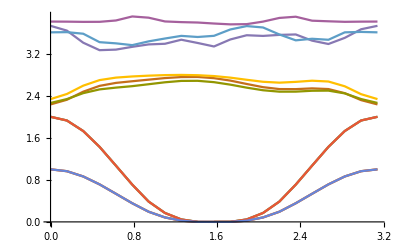

```mathematica
ListLinePlot[{tm4max,tm4mean,tmmax,tmmean,tm16max,tm16mean,tm32max,tm32mean,tm64max,tm64mean,alttmmax,alttmmean}]
```

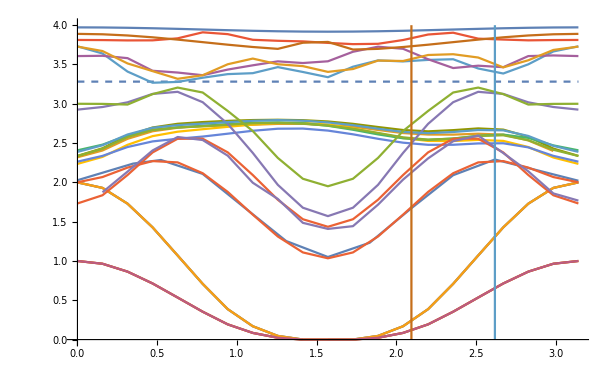

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],ListLinePlot[{fitvals,fitvals16n,tm4max,tm4mean,tmmax,tmmean,tm16max,tm16mean,tm32max,tm32mean,tm64max,tm64mean,alttmmax,alttmmean,rd64mean,rd64max,rd16max,rd16mean,rdmean,rdnmax,rd32max,rd32mean,fibo16max,fibo16mean,fibo32max,fibo32mean,fibo64max,fibo64mean,fibomax,fibomean,altfibomax,altfibomean,altrdmax,altrdmean,alternatefitvals2,{{2.0943951023931953,0},{2.0943951023931953,4}},{{5Pi/6,0},{5Pi/6,4}}}],PlotRange->All]
```

```mathematica
N[2*180/7]
```

51.4286

## dt = pi/2

#### data

## allplots

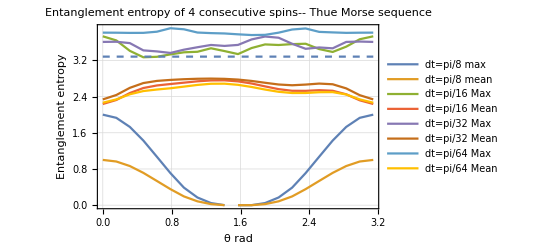

```mathematica
Show[ListLinePlot[{tmmax,tmmean,tm16max,tm16mean,tm32max,tm32mean,tm64max,tm64mean},PlotTheme->"Detailed",PlotLegends->Placed[{"dt=pi/8 max","dt=pi/8 mean ","dt=pi/16 Max","dt=pi/16 Mean","dt=pi/32 Max","dt=pi/32 Mean","dt=pi/64 Max","dt=pi/64 Mean"},{0.5,0.47}]],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],PlotRange->All,FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[θ rad],None}},PlotLabel->HoldForm[Entanglement entropy of 4 consecutive spins -- Thue Morse sequence],LabelStyle->{FontFamily->"TeX Gyre Pagella",RGBColor[0.,0.,0.]},LabelStyle->{17,GrayLevel[0]}]
```

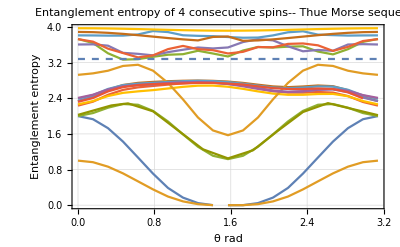

```mathematica
Show[ListLinePlot[{tmmax,tmmean,tm16max,tm16mean,tm32max,tm32mean,tm64max,tm64mean,fibomax,fibomean,fibo16max,fibo16mean,fibo32max,fibo32mean,fibo64max,fibo64mean,rdnmax,rdmean,rd16max,rd16mean,rd32max,rd32mean,rd64max,rd64mean,fitvals,fitvals16n},PlotTheme->"Detailed"],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],PlotRange->All,FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[θ rad],None}},PlotLabel->HoldForm[Entanglement entropy of 4 consecutive spins -- Thue Morse sequence],LabelStyle->{FontFamily->"TeX Gyre Pagella",RGBColor[0.,0.,0.]},LabelStyle->{17,GrayLevel[0]}]
```

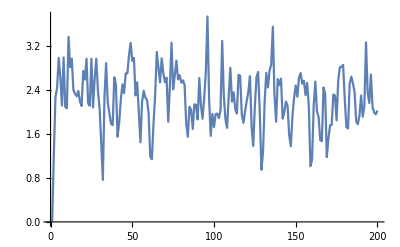

```mathematica
ListLinePlot[tm16n[[1]]]
```

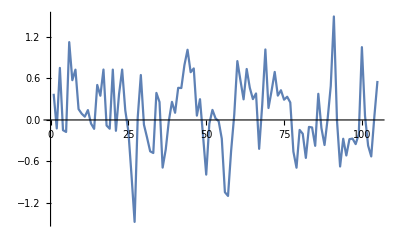

```mathematica
ListLinePlot[Table[Drop[tm16n[[1]],5][[n]]-tm16mean[[1]][[2]],{n,1,105}]]
```

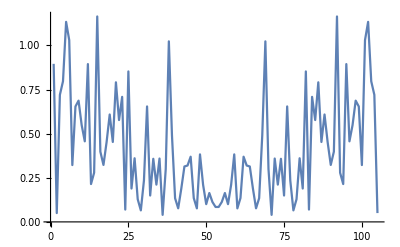

```mathematica
ListLinePlot[Abs[Fourier[Table[Drop[tm16n[[1]],5][[n]]-tm16mean[[1]][[2]],{n,1,105}]]],PlotRange->All]
```

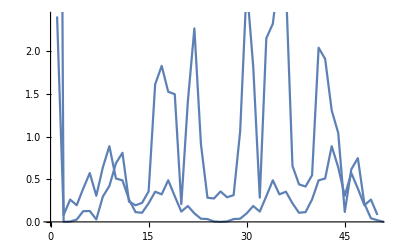

```mathematica
Show[ListLinePlot[Abs[Fourier[Drop[tm025pi,150]]],PlotRange->All],ListLinePlot[Abs[Fourier[tm005pi]],PlotRange->All]]
```

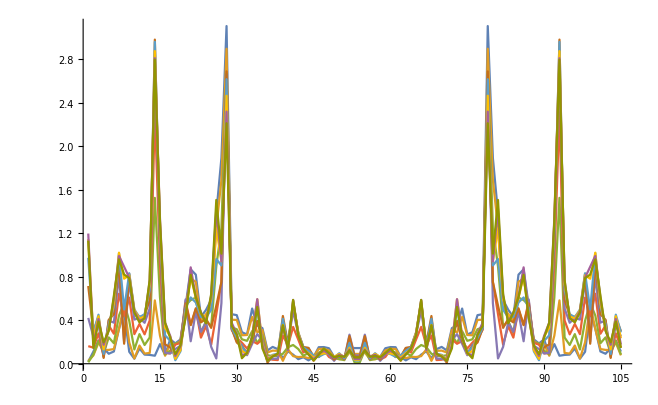

```mathematica
ListLinePlot[Table[Abs[Fourier[Table[Drop[tm64n[[m]],5][[n]]-tm64mean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All]
```

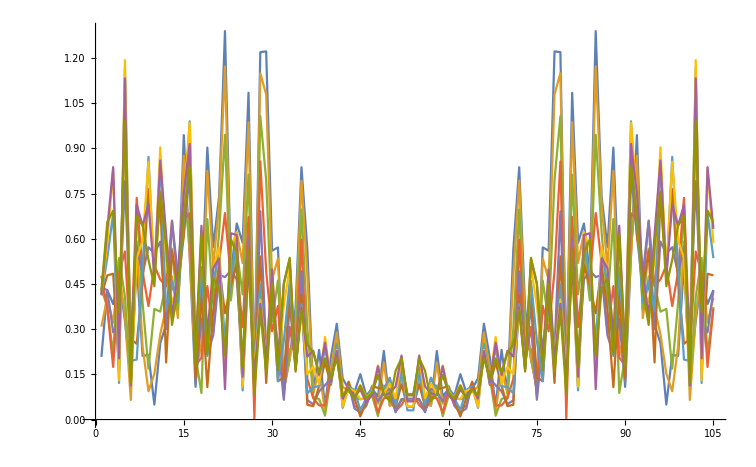

```mathematica
ListLinePlot[Table[Abs[Fourier[Table[Drop[tm32n[[m]],5][[n]]-tm32mean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All]
```

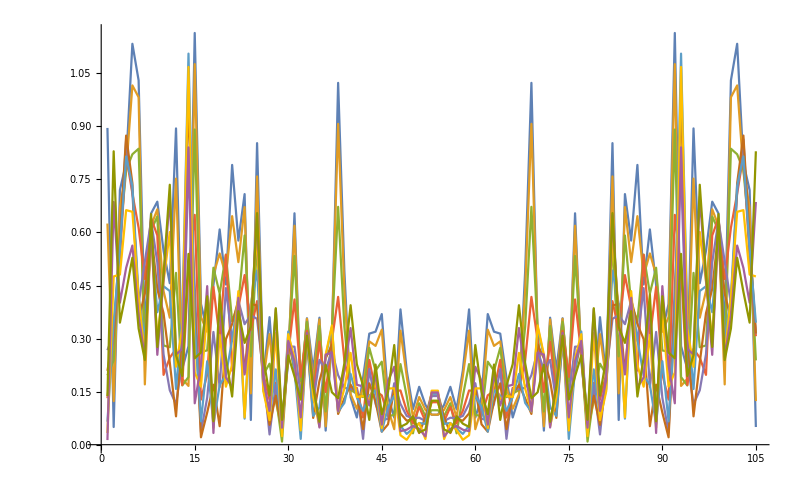

```mathematica
ListLinePlot[Table[Abs[Fourier[Table[Drop[tm16n[[m]],5][[n]]-tm16mean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All]
```

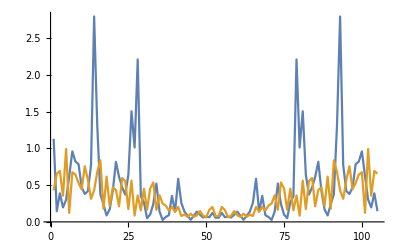

```mathematica
ListLinePlot[{Abs[Fourier[Table[Drop[tm64n[[10]],5][[n]]-tm64mean[[10]][[2]],{n,1,105}]]],Abs[Fourier[Table[Drop[tm32n[[10]],5][[n]]-tm32mean[[10]][[2]],{n,1,105}]]]},PlotRange->All]
```

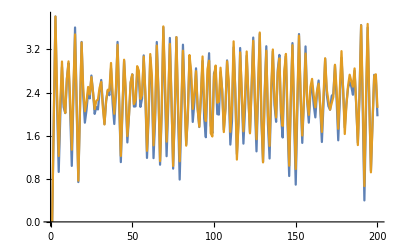

```mathematica
ListLinePlot[{tm64n[[1]],tm64n[[2]]}]
```

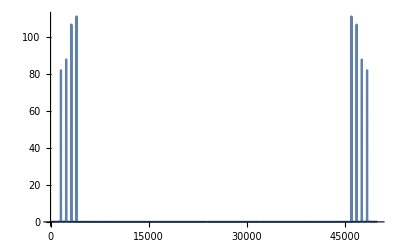

```mathematica
ListLinePlot[Abs[Fourier[Table[Sin[4x]+Sin[5x]+Sin[3x]+Sin[2x],{x,0,5000,0.1}]]],PlotRange->All]
```

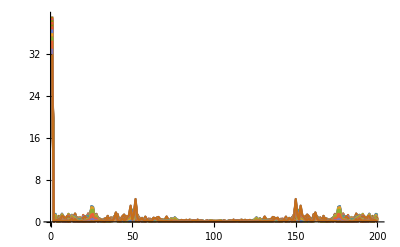

```mathematica
Show[ListLinePlot[Table[Abs[Fourier[tm32n[[n]]]],{n,1,21}],PlotRange->All],ListLinePlot[Table[Abs[Fourier[tm16n[[n]]]],{n,1,21}],PlotRange->All],ListLinePlot[Table[Abs[Fourier[tm64n[[n]]]],{n,1,21}],PlotRange->All]]
```

## ok -- alternate elements of sequence of sum of thue morse series form thue morse series...!

```mathematica
sums=Table[Sum[ThueMorse[n],{n,0,m}],{m,0,100}]
```

{0,1,2,2,3,3,3,4,5,5,5,6,6,7,8,8,9,9,9,10,10,11,12,12,12,13,14,14,15,15,15,16,17,17,17,18,18,19,20,20,20,21,22,22,23,23,23,24,24,25,26,26,27,27,27,28,29,29,29,30,30,31,32,32,33,33,33,34,34,35,36,36,36,37,38,38,39,39,39,40,40,41,42,42,43,43,43,44,45,45,45,46,46,47,48,48,48,49,50,50,51}

```mathematica
Drop[sums,{2,100,2}]
```

{0,2,3,3,5,5,6,8,9,9,10,12,12,14,15,15,17,17,18,20,20,22,23,23,24,26,27,27,29,29,30,32,33,33,34,36,36,38,39,39,40,42,43,43,45,45,46,48,48,50,51}

```mathematica
Table[(-1)^ThueMorse[n],{n,0,50}]
```

{1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,1,-1,-1}

## kicked interaction term

## dt = pi/8 after*kick

#### data

```mathematica
datatm8={-0.000000000000000000*10^+00,1.201752073385712993*10^+00,-4.484797105340891600*10^-15,1.201752073385712993*10^+00,-7.688223609155823637*10^-15,1.201752073385712105*10^+00,-1.153233541373374966*10^-14,1.201752073385710773*10^+00,-1.601713251907467518*10^-14,1.201752073385710773*10^+00,-1.857987372212664163*10^-14,1.201752073385709441*10^+00,-2.114261492517861124*10^-14,1.201752073385708997*10^+00,-2.306467082746759082*10^-14,1.201752073385709663*10^+00,-2.306467082746759082*10^-14,1.201752073385709663*10^+00,-2.306467082746759082*10^-14,1.201752073385708774*10^+00,-2.434604142899358036*10^-14,1.201752073385708774*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385709441*10^+00,-2.434604142899358036*10^-14,1.201752073385708774*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,-2.562741203051956674*10^-14,1.201752073385708552*10^+00,-2.626809733128256624*10^-14,1.201752073385708997*10^+00,-2.562741203051956674*10^-14,1.201752073385708997*10^+00,-2.498672672975657355*10^-14,1.201752073385708552*10^+00,2.722912528242654327*10^-14,1.157960598926154105*10^+00,2.370535612823019905*10^-14,1.201752073385714548*10^+00,2.338501347784871034*10^-14,1.201752073385712549*10^+00,2.066210094960607053*10^-14,1.157960598926152773*10^+00,1.361456264121333632*10^-14,1.201752073385710773*10^+00,1.121199276335216944*10^-14,1.157960598926151663*10^+00,6.406853007629821477*10^-15,1.157960598926150553*10^+00,3.523769154196404968*10^-15,1.201752073385709219*10^+00,-9.610279511444755881*10^-16,1.201752073385708330*10^+00,-4.164454454959398948*10^-15,1.157960598926147666*10^+00,-7.047538308392836756*10^-15,1.157960598926147222*10^+00,-8.969594210681797399*10^-15,1.201752073385707220*10^+00,-1.313404866564122317*10^-14,1.157960598926146778*10^+00,-1.633747516945617335*10^-14,1.201752073385705888*10^+00,-1.922055902288963482*10^-14,1.201752073385705222*10^+00,-2.306467082746759082*10^-14,1.157960598926143891*10^+00,-2.883083853433454532*10^-14,1.201752073385704334*10^+00,-3.299529298929403420*10^-14,1.157960598926142559*10^+00,-3.683940479387202490*10^-14,1.157960598926141893*10^+00,-4.100385924883153271*10^-14,1.201752073385702335*10^+00,-4.548865635417254501*10^-14,1.157960598926140117*10^+00,-5.125482406103959418*10^-14,1.201752073385700115*10^+00,-5.445825056485463271*10^-14,1.201752073385699671*10^+00,-5.862270501981418470*10^-14,1.157960598926137674*10^+00,-6.214647417401074665*10^-14,1.157960598926137674*10^+00,-6.631092862897031757*10^-14,1.201752073385697894*10^+00,-6.759229923049634813*10^-14,1.201752073385698338*10^+00,-6.887366983202237869*10^-14,1.157960598926135454*10^+00,-7.431949488850800541*10^-14,1.201752073385696562*10^+00,-7.752292139232308812*10^-14,1.157960598926133677*10^+00,-8.328908909919026981*10^-14,1.157960598926132789*10^+00,-8.937559945643898124*10^-14,1.201752073385694120*10^+00,-9.289936861063560630*10^-14,1.201752073385693231*10^+00,-9.610279511445072687*10^-14,1.157960598926131235*10^+00,-1.018689628213179843*10^-13,1.157960598926129681*10^+00,-1.076351305281852417*10^-13,1.201752073385691455*10^+00,-1.095571864304743444*10^-13,1.157960598926128126*10^+00,-1.153233541373416396*10^-13,1.201752073385689235*10^+00,-1.198081512426829044*10^-13,1.201752073385689457*10^+00,-1.226912350961165457*10^-13,1.157960598926125684*10^+00,-1.281370601526023996*10^-13,1.157960598926124796*10^+00,-1.323015146075621851*10^-13,1.201752073385687458*10^+00,-1.371066543632849796*10^-13,1.201752073385686348*10^+00,-1.412711088182447903*10^-13,1.157960598926122575*10^+00,-1.447948779724415416*10^-13,1.201752073385684794*10^+00,-1.489593324274013523*10^-13,1.157960598926120799*10^+00,-1.524831015815981288*10^-13,1.157960598926120355*10^+00,-1.560068707357949306*10^-13,1.201752073385683239*10^+00,-1.592102972396102026*10^-13,1.157960598926119244*10^+00,-1.636950943449515936*10^-13,1.201752073385681685*10^+00,-1.672188634991483954*10^-13,1.201752073385681241*10^+00,-1.720240032548713413*10^-13,1.157960598926117024*10^+00,-1.784308562625019358*10^-13,1.201752073385679465*10^+00,-1.825953107174618475*10^-13,1.157960598926114804*10^+00,-1.880411357739479287*10^-13,1.157960598926113693*10^+00,-1.918852475785263359*10^-13,1.201752073385676800*10^+00,-1.954090167327231881*10^-13,1.201752073385676134*10^+00,-1.979717579357755017*10^-13,1.157960598926112139*10^+00,-2.027768976914985486*10^-13,1.157960598926111251*10^+00,-2.066210094960769810*10^-13,1.201752073385674580*10^+00,-2.098244359998923793*10^-13,1.157960598926109697*10^+00,-2.146295757556154514*10^-13,1.201752073385672803*10^+00,-2.175126596090492947*10^-13,1.201752073385672803*10^+00,-2.200754008121016335*10^-13,1.157960598926107476*10^+00,-2.239195126166801417*10^-13,1.201752073385672359*10^+00,-2.264822538197324553*10^-13,1.157960598926106144*10^+00,-2.312873935754555779*10^-13,1.157960598926105700*10^+00,-2.357721906807971960*10^-13,1.201752073385669473*10^+00,-2.396163024853757042*10^-13,1.157960598926104145*10^+00,-2.428197289891911530*10^-13,1.201752073385668140*10^+00,-2.469841834441512666*10^-13,1.201752073385667918*10^+00,-2.514689805494929353*10^-13,1.157960598926101703*10^+00,-2.556334350044530489*10^-13,1.157960598926101259*10^+00,-2.607589174105578780*10^-13,1.201752073385665254*10^+00,-2.646030292151364367*10^-13,1.201752073385665254*10^+00,-2.662047424670442115*10^-13,1.157960598926099260*10^+00,-2.687674836700966513*10^-13,1.201752073385664144*10^+00,-2.706895395723859306*10^-13,1.157960598926098372*10^+00,-2.770963925800169796*10^-13,1.157960598926097706*10^+00,-2.822218749861218591*10^-13,1.201752073385661701*10^+00,-2.851049588395558539*10^-13,1.157960598926095264*10^+00,-2.908711265464238938*10^-13,1.201752073385660369*10^+00,-2.953559236517656634*10^-13,1.201752073385659259*10^+00,-2.992000354563443231*10^-13,1.157960598926092599*10^+00,-3.036848325616861432*10^-13,1.201752073385658370*10^+00,-3.062475737647386334*10^-13,1.157960598926091489*10^+00,-3.123340841219882789*10^-13,1.157960598926090157*10^+00,-3.184205944792379748*10^-13,1.201752073385655928*10^+00,-3.216240209830535750*10^-13,1.201752073385655484*10^+00,-3.251477901372507807*10^-13,1.157960598926088602*10^+00,-3.280308739906848259*10^-13,1.157960598926087714*10^+00,-3.337970416975530678*10^-13,1.201752073385653485*10^+00,-3.366801255509871130*10^-13,1.157960598926085272*10^+00,-3.440480065097631803*10^-13,1.201752073385651709*10^+00,-3.469310903631972760*10^-13,1.201752073385651487*10^+00,-3.507752021677761376*10^-13,1.157960598926083273*10^+00,-3.555803419234996642*10^-13,1.157960598926082607*10^+00,-3.616668522807495620*10^-13,1.201752073385649044*10^+00,-3.645499361341837082*10^-13,1.201752073385647712*10^+00,-3.687143905891441248*10^-13,1.157960598926080165*10^+00,-3.725585023937230369*10^-13,1.201752073385646380*10^+00,-3.764026141983018985*10^-13,1.157960598926078388*10^+00,-3.808874113036440215*10^-13,1.157960598926077500*10^+00,-3.860128937097492545*10^-13,1.201752073385644159*10^+00,-3.908180334654728820*10^-13,1.201752073385643937*10^+00,-3.949824879204333995*10^-13,1.157960598926075502*10^+00,-3.965842011723413259*10^-13,1.157960598926075502*10^+00,-3.991469423753939676*10^-13,1.201752073385641939*10^+00,-4.036317394807360906*10^-13,1.157960598926073725*10^+00,-4.058741380334071773*10^-13,1.201752073385641051*10^+00,-4.103589351387493003*10^-13,1.201752073385640607*10^+00,-4.138827042929467584*10^-13,1.157960598926072171*10^+00,-4.183675013982889319*10^-13,1.201752073385638386*10^+00,-4.215709279021047846*10^-13,1.157960598926070839*10^+00,-4.263760676578285635*10^-13,1.157960598926069951*10^+00,-4.311812074135523425*10^-13,1.201752073385636610*10^+00,-4.331032633158418743*10^-13,1.157960598926068840*10^+00,-4.382287457219473092*10^-13,1.201752073385635278*10^+00,-4.414321722257631618*10^-13,1.201752073385635278*10^+00,-4.433542281280527441*10^-13,1.157960598926065954*10^+00,-4.488000531845397340*10^-13,1.157960598926065510*10^+00,-4.532848502898820589*10^-13,1.201752073385633279*10^+00,-4.552069061921715402*10^-13,1.201752073385632613*10^+00,-4.584103326959875948*10^-13,1.157960598926063511*10^+00,-4.657782136547641669*10^-13,1.201752073385630837*10^+00,-4.702630107601065424*10^-13,1.157960598926060847*10^+00,-4.769902064181201055*10^-13,1.157960598926059737*10^+00,-4.827563741249889028*10^-13,1.201752073385628172*10^+00,-4.856394579784233015*10^-13,1.201752073385627950*10^+00,-4.882021991814760442*10^-13,1.157960598926057738*10^+00,-4.942887095387264974*10^-13,1.157960598926056184*10^+00,-5.000548772455953956*10^-13,1.201752073385625286*10^+00,-5.032583037494113493*10^-13,1.157960598926054852*10^+00,-5.090244714562802475*10^-13,1.201752073385624175*10^+00,-5.115872126593330912*10^-13,1.201752073385623509*10^+00,-5.141499538623859349*10^-13,1.157960598926053075*10^+00,-5.192754362684916222*10^-13,1.157960598926052631*10^+00,-5.240805760242156536*10^-13,1.201752073385621511*10^+00,-5.276043451784134651*10^-13,1.201752073385620623*10^+00,-5.314484569829927306*10^-13,1.157960598926050189*10^+00,-5.340111981860456752*10^-13,1.201752073385619290*10^+00,-5.378553099906249407*10^-13,1.157960598926048856*10^+00,-5.439418203478755959*10^-13,1.157960598926047746*10^+00,-5.490673027539813842*10^-13,1.201752073385617514*10^+00,-5.529114145585607507*10^-13,1.157960598926046636*10^+00,-5.577165543142849841*10^-13,1.201752073385615294*10^+00,-5.609199808181011396*10^-13,1.201752073385615294*10^+00,-5.644437499722989511*10^-13,1.157960598926043971*10^+00,-5.705302603295496063*10^-13,1.201752073385613961*10^+00,-5.724523162318394410*10^-13,1.157960598926042195*10^+00,-5.791795118898534081*10^-13,1.157960598926041307*10^+00,-5.852660222471041642*10^-13,1.201752073385611519*10^+00,-5.878287634501571089*10^-13,1.201752073385611075*10^+00,-5.900711620028284985*10^-13,1.157960598926038642*10^+00,-5.974390429616058785*10^-13,1.157960598926037532*10^+00,-6.044865812700016024*10^-13,1.201752073385608410*10^+00,-6.064086371722913362*10^-13,1.157960598926035534*10^+00,-6.137765181310688171*10^-13,1.201752073385606412*10^+00,-6.166596019845034177*10^-13,1.201752073385606190*10^+00,-6.198630284883197752*10^-13,1.157960598926033979*10^+00,-6.249885108944257654*10^-13,1.157960598926032869*10^+00,-6.297936506501503017*10^-13,1.201752073385604191*10^+00,-6.349191330562563929*10^-13,1.201752073385602859*10^+00,-6.390835875112176173*10^-13,1.157960598926029760*10^+00,-6.438887272669421536*10^-13,1.201752073385601527*10^+00,-6.461311258196136442*10^-13,1.157960598926028872*10^+00,-6.499752376241932126*10^-13,1.157960598926028206*10^+00,-6.538193494287727811*10^-13,1.201752073385599751*10^+00,-6.570227759325892396*10^-13,1.201752073385598862*10^+00,-6.611872303875505649*10^-13,1.157960598926025764*10^+00,-6.675940833951832799*10^-13,1.157960598926024876*10^+00,-6.730399084516712291*10^-13,1.201752073385596420*10^+00,-6.762433349554875866*10^-13,1.157960598926023765*10^+00,-6.797671041096857010*10^-13,1.201752073385595754*10^+00,-6.842519012150286823*10^-13,1.201752073385594866*10^+00,-6.903384115722798423*10^-13,1.157960598926020879*10^+00,-6.941825233768597137*10^-13,1.201752073385592645*10^+00,-7.009097190348741856*10^-13,1.157960598926018436*10^+00,-7.076369146928888595*10^-13,1.157960598926017770*10^+00,-7.118013691478502858*10^-13,1.201752073385589537*10^+00,-7.150047956516667443*10^-13,1.157960598926015994*10^+00,-7.198099354073915835*10^-13,1.201752073385588870*10^+00,-7.233337045615897989*10^-13,1.201752073385588204*10^+00,-7.268574737157879133*10^-13,1.157960598926014217*10^+00,-7.316626134715127525*10^-13,1.157960598926012885*10^+00,-7.364677532272374907*10^-13,1.201752073385585540*10^+00,-7.412728929829624309*10^-13,1.201752073385585096*10^+00,-7.444763194867789903*10^-13,1.157960598926010665*10^+00,-7.470390606898322379*10^-13,1.201752073385584207*10^+00,-7.528052283967020449*10^-13,1.157960598926009332*10^+00,-7.563289975509003613*10^-13,1.157960598926008666*10^+00,-7.595324240547169208*10^-13,1.201752073385582653*10^+00,-7.614544799570068564*10^-13,1.157960598926007334*10^+00,-7.672206476638768654*10^-13,1.201752073385580655*10^+00,-7.701037315173117689*10^-13,1.201752073385580211*10^+00,-7.726664727203650165*10^-13,1.157960598926005780*10^+00,-7.761902418745634338*10^-13,1.201752073385579100*10^+00,-7.800343536791433052*10^-13,1.157960598926003781*10^+00,-7.835581228333417225*10^-13,1.157960598926002893*10^+00,-7.877225772883033508*10^-13,1.201752073385577102*10^+00,-7.912463464425016672*10^-13,1.201752073385577102*10^+00,-7.944497729463183276*10^-13,1.157960598926000895*10^+00,-8.018176539050967173*10^-13,1.157960598925999562*10^+00,-8.088651922134934510*10^-13,1.201752073385573993*10^+00,-8.107872481157834877*10^-13,1.157960598925998230*10^+00,-8.146313599203635610*10^-13,1.201752073385572883*10^+00,-8.184754717249436343*10^-13,1.201752073385572661*10^+00,-8.226399261799054645*10^-13,1.157960598925996232*10^+00,-8.258433526837221249*10^-13,1.201752073385570663*10^+00,-8.309688350898289230*10^-13,1.157960598925994011*10^+00,-8.354536321951724091*10^-13,1.157960598925993345*10^+00,-8.383367160486075146*10^-13,1.201752073385568664*10^+00,-8.412197999020426201*10^-13,1.157960598925992679*10^+00,-8.473063102592944869*10^-13,1.201752073385567110*10^+00,-8.508300794134930052*10^-13,1.201752073385566888*10^+00,-8.546741912180731795*10^-13,1.157960598925990237*10^+00,-8.601200162745617345*10^-13,1.157960598925989126*10^+00,-8.652454986806687345*10^-13,1.201752073385564445*10^+00,-8.674878972333405281*10^-13,1.201752073385564001*10^+00,-8.729337222898291840*10^-13,1.157960598925987128*10^+00,-8.783795473463178400*10^-13,1.201752073385562447*10^+00,-8.815829738501347023*10^-13,1.157960598925984907*10^+00,-8.883101695081501840*10^-13,1.157960598925984463*10^+00,-8.943966798654022528*10^-13,1.201752073385559783*10^+00,-8.972797637188374593*10^-13,1.201752073385558894*10^+00,-9.020849034745628033*10^-13,1.157960598925981355*10^+00,-9.068900432302882484*10^-13,1.157960598925980245*10^+00,-9.116951829860136934*10^-13,1.201752073385556674*10^+00,-9.158596374409756246*10^-13,1.157960598925979356*10^+00,-9.197037492455558998*10^-13,1.201752073385555786*10^+00,-9.251495743020448587*10^-13,1.201752073385554898*10^+00,-9.273919728547166523*10^-13,1.157960598925977358*10^+00,-9.331581405615872671*10^-13,1.157960598925975360*10^+00,-9.382836229676945700*10^-13,1.201752073385552677*10^+00,-9.408463641707480195*10^-13,1.201752073385551789*10^+00,-9.440497906745651848*10^-13,1.157960598925973805*10^+00,-9.491752730806722858*10^-13,1.201752073385549568*10^+00,-9.523786995844892492*10^-13,1.157960598925972029*10^+00,-9.575041819905967540*10^-13,1.157960598925971141*10^+00,-9.619889790959403412*10^-13,1.201752073385548236*10^+00,-9.648720629493758505*10^-13,1.157960598925970030*10^+00,-9.712789159570099792*10^-13,1.201752073385546904*10^+00,-9.751230277615906583*10^-13,1.201752073385546460*10^+00,-9.780061116150259657*10^-13,1.157960598925967810*10^+00,-9.828112513707514108*10^-13,1.201752073385545128*10^+00,-9.856943352241869201*10^-13,1.157960598925965590*10^+00,-9.908198176302944250*10^-13,1.157960598925964701*10^+00,-9.937029014837297324*10^-13,1.201752073385542685*10^+00,-9.975470132883102096*10^-13,1.201752073385542019*10^+00,-1.000430097141745517*10^-12,1.157960598925962925*10^+00,-9.610279511444755881*10^-16,1.033390542523311195*10^+00,1.601713251907458574*10^-16,1.201752073385713437*10^+00,-1.281370601525967648*10^-15,1.201752073385713215*10^+00,-4.484797105340891600*10^-15,1.033390542523308975*10^+00,-9.930622161826277720*10^-15,1.201752073385711661*10^+00,-1.665781781983766837*10^-14,1.033390542523306088*10^+00,-2.082227227479711307*10^-14,1.033390542523305866*10^+00,-2.466638407937507853*10^-14,1.201752073385709663*10^+00,-3.075289443662354067*10^-14,1.201752073385708552*10^+00,-3.619871949310902225*10^-14,1.033390542523302313*10^+00,-4.068351659845002823*10^-14,1.033390542523301425*10^+00,-4.484797105340954235*10^-14,1.201752073385705444*10^+00,-4.997345345951358255*10^-14,1.033390542523299427*10^+00,-5.349722261371011295*10^-14,1.201752073385704556*10^+00,-5.766167706866967124*10^-14,1.201752073385703667*10^+00,-6.150578887324773768*10^-14,1.033390542523295874*10^+00,-6.374818742591826907*10^-14,1.201752073385703223*10^+00,-6.727195658011484364*10^-14,1.033390542523294986*10^+00,-7.079572573431141822*10^-14,1.033390542523294542*10^+00,-7.431949488850800541*10^-14,1.201752073385701225*10^+00,-7.848394934346761419*10^-14,1.033390542523292321*10^+00,-8.328908909919026981*10^-14,1.201752073385699227*10^+00,-8.649251560300537777*10^-14,1.201752073385699227*10^+00,-9.001628475720199021*10^-14,1.033390542523289435*10^+00,-9.546210981368770528*10^-14,1.033390542523288325*10^+00,-1.002672495694104114*10^-13,1.201752073385696562*10^+00,-1.018689628213179843*10^-13,1.201752073385696118*10^+00,-1.041113613739885788*10^-13,1.033390542523286992*10^+00,-1.079554731785667588*10^-13,1.201752073385695452*10^+00,-1.098775290808558615*10^-13,1.033390542523284772*10^+00,-1.140419835358155712*10^-13,1.033390542523284328*10^+00,-1.175657526900122720*10^-13,1.201752073385694120*10^+00,-1.207691791938274431*10^-13,1.201752073385693675*10^+00,-1.226912350961165457*10^-13,1.033390542523281441*10^+00,-1.274963748518393402*10^-13,1.033390542523280775*10^+00,-1.310201440060360662*10^-13,1.201752073385691677*10^+00,-1.332625425587067491*10^-13,1.033390542523279443*10^+00,-1.374269970136665345*10^-13,1.201752073385690567*10^+00,-1.409507661678632858*10^-13,1.201752073385689679*10^+00,-1.444745353220600119*10^-13,1.033390542523276778*10^+00,-1.479983044762567884*10^-13,1.033390542523275890*10^+00,-1.508813883296905054*10^-13,1.201752073385688124*10^+00,-1.550458427846503414*10^-13,1.201752073385687680*10^+00,-1.588899545892286729*10^-13,1.033390542523273448*10^+00,-1.640154369953331233*10^-13,1.201752073385686126*10^+00,-1.697816047022006332*10^-13,1.033390542523271671*10^+00,-1.733053738563974602*10^-13,1.033390542523271005*10^+00,-1.787511989128834656*10^-13,1.201752073385683461*10^+00,-1.838766813189879917*10^-13,1.033390542523268563*10^+00,-1.877207931235663989*10^-13,1.201752073385681907*10^+00,-1.922055902289078656*10^-13,1.201752073385680797*10^+00,-1.976514152853939720*10^-13,1.033390542523265676*10^+00,-2.008548417892093197*10^-13,1.201752073385679909*10^+00,-2.053396388945508369*10^-13,1.033390542523263234*10^+00,-2.095040933495108243*10^-13,1.033390542523262345*10^+00,-2.143092331052338965*10^-13,1.201752073385677466*10^+00,-2.187940302105754641*10^-13,1.201752073385676800*10^+00,-2.242398552670616714*10^-13,1.033390542523258793*10^+00,-2.280839670716401796*10^-13,1.033390542523258571*10^+00,-2.312873935754555779*10^-13,1.201752073385674358*10^+00,-2.344908200792710266*10^-13,1.033390542523256572*10^+00,-2.373739039327049709*10^-13,1.201752073385673469*10^+00,-2.402569877861388142*10^-13,1.201752073385673247*10^+00,-2.431400716395727584*10^-13,1.033390542523254130*10^+00,-2.463434981433882072*10^-13,1.201752073385672581*10^+00,-2.495469246472036559*10^-13,1.033390542523252353*10^+00,-2.540317217525453245*10^-13,1.033390542523251909*10^+00,-2.588368615082685986*10^-13,1.201752073385669917*10^+00,-2.633216586136102673*10^-13,1.033390542523250133*10^+00,-2.681267983693335413*10^-13,1.201752073385668140*10^+00,-2.726115954746752605*10^-13,1.201752073385668140*10^+00,-2.764557072792538696*10^-13,1.033390542523247024*10^+00,-2.809405043845956392*10^-13,1.033390542523245914*10^+00,-2.857456441403189638*10^-13,1.201752073385665476*10^+00,-2.902304412456607334*10^-13,1.201752073385665032*10^+00,-2.937542103998578886*10^-13,1.033390542523242805*10^+00,-2.979186648548181032*10^-13,1.201752073385663699*10^+00,-3.017627766593968134*10^-13,1.033390542523240585*10^+00,-3.059272311143570785*10^-13,1.033390542523240141*10^+00,-3.100916855693173436*10^-13,1.201752073385661257*10^+00,-3.132951120731329943*10^-13,1.033390542523238365*10^+00,-3.168188812273301495*10^-13,1.201752073385660591*10^+00,-3.203426503815273551*10^-13,1.201752073385659925*10^+00,-3.229053915845798454*10^-13,1.033390542523236366*10^+00,-3.267495033891586060*10^-13,1.201752073385658814*10^+00,-3.309139578441189216*10^-13,1.033390542523234590*10^+00,-3.331563563967899074*10^-13,1.033390542523233258*10^+00,-3.373208108517502735*10^-13,1.201752073385656816*10^+00,-3.405242373555659242*10^-13,1.201752073385656372*10^+00,-3.430869785586184649*10^-13,1.033390542523231037*10^+00,-3.469310903631972760*10^-13,1.033390542523229483*10^+00,-3.520565727693024080*10^-13,1.201752073385654596*10^+00,-3.549396566227365542*10^-13,1.033390542523228151*10^+00,-3.597447963784601312*10^-13,1.201752073385653041*10^+00,-3.619871949311311170*10^-13,1.201752073385652597*10^+00,-3.658313067357099786*10^-13,1.033390542523225264*10^+00,-3.719178170929598765*10^-13,1.033390542523224376*10^+00,-3.783246701005913798*10^-13,1.201752073385650155*10^+00,-3.824891245555518974*10^-13,1.201752073385649489*10^+00,-3.869739216608939699*10^-13,1.033390542523220157*10^+00,-3.927400893677623633*10^-13,1.201752073385647712*10^+00,-3.981859144242492522*10^-13,1.033390542523218159*10^+00,-4.023503688792097697*10^-13,1.033390542523217714*10^+00,-4.058741380334071773*10^-13,1.201752073385645270*10^+00,-4.097182498379861904*10^-13,1.201752073385644826*10^+00,-4.151640748944730288*10^-13,1.033390542523214384*10^+00,-4.209302426013416242*10^-13,1.033390542523213274*10^+00,-4.247743544059205867*10^-13,1.201752073385642161*10^+00,-4.308608647631707875*10^-13,1.033390542523211497*10^+00,-4.331032633158418743*10^-13,1.201752073385641051*10^+00,-4.369473751204209378*10^-13,1.201752073385640163*10^+00,-4.414321722257631618*10^-13,1.033390542523208833*10^+00,-4.449559413799606704*10^-13,1.201752073385639275*10^+00,-4.494407384853029449*10^-13,1.033390542523206168*10^+00,-4.529645076395004535*10^-13,1.033390542523205946*10^+00,-4.571289620944611730*10^-13,1.201752073385637054*10^+00,-4.609730738990403375*10^-13,1.033390542523203726*10^+00,-4.680206122074354556*10^-13,1.201752073385635722*10^+00,-4.715443813616328632*10^-13,1.201752073385634390*10^+00,-4.769902064181201055*10^-13,1.033390542523201061*10^+00,-4.795529476211729492*10^-13,1.033390542523200395*10^+00,-4.840377447265152237*10^-13,1.201752073385632391*10^+00,-4.875615138807128332*10^-13,1.201752073385631947*10^+00,-4.914056256852920988*10^-13,1.033390542523197730*10^+00,-4.962107654410160292*10^-13,1.201752073385630393*10^+00,-4.994141919448320838*10^-13,1.033390542523196176*10^+00,-5.029379610990296933*10^-13,1.033390542523195066*10^+00,-5.071024155539906148*10^-13,1.201752073385628616*10^+00,-5.106261847081882243*10^-13,1.201752073385628172*10^+00,-5.138296112120042789*10^-13,1.033390542523191957*10^+00,-5.179940656669652004*10^-13,1.033390542523191513*10^+00,-5.215178348211628099*10^-13,1.201752073385626174*10^+00,-5.256822892761237314*10^-13,1.033390542523189737*10^+00,-5.285653731295582310*10^-13,1.201752073385625064*10^+00,-5.320891422837559415*10^-13,1.201752073385624175*10^+00,-5.368942820394801749*10^-13,1.033390542523186850*10^+00,-5.413790791448226513*10^-13,1.033390542523186184*10^+00,-5.452231909494020178*10^-13,1.201752073385622399*10^+00,-5.503486733555078061*10^-13,1.201752073385621067*10^+00,-5.548334704608503835*10^-13,1.033390542523183075*10^+00,-5.577165543142849841*10^-13,1.201752073385619735*10^+00,-5.618810087692460065*10^-13,1.033390542523181077*10^+00,-5.644437499722989511*10^-13,1.033390542523180855*10^+00,-5.673268338257334507*10^-13,1.201752073385618624*10^+00,-5.711709456303128172*10^-13,1.033390542523179301*10^+00,-5.766167706868003624*10^-13,1.201752073385616848*10^+00,-5.814219104425247977*10^-13,1.201752073385615960*10^+00,-5.862270501982490311*10^-13,1.033390542523175526*10^+00,-5.900711620028284985*10^-13,1.201752073385614406*10^+00,-5.951966444089344888*10^-13,1.033390542523173750*10^+00,-6.006424694654221350*10^-13,1.033390542523172639*10^+00,-6.044865812700016024*10^-13,1.201752073385612185*10^+00,-6.083306930745810699*10^-13,1.201752073385611963*10^+00,-6.118544622287790834*10^-13,1.033390542523169309*10^+00,-6.153782313829769958*10^-13,1.033390542523168865*10^+00,-6.192223431875564633*10^-13,1.201752073385609521*10^+00,-6.214647417402278530*10^-13,1.033390542523167088*10^+00,-6.249885108944257654*10^-13,1.201752073385609076*10^+00,-6.281919373982421229*10^-13,1.201752073385608188*10^+00,-6.320360492028216914*10^-13,1.033390542523164868*10^+00,-6.349191330562563929*10^-13,1.033390542523163980*10^+00,-6.384429022104543054*10^-13,1.201752073385606190*10^+00,-6.438887272669421536*10^-13,1.201752073385605302*10^+00,-6.474124964211400661*10^-13,1.033390542523161093*10^+00,-6.502955802745748686*10^-13,1.201752073385604636*10^+00,-6.551007200302994049*10^-13,1.033390542523159317*10^+00,-6.583041465341157624*10^-13,1.033390542523159095*10^+00,-6.624686009890770877*10^-13,1.201752073385602193*10^+00,-6.656720274928934452*10^-13,1.201752073385601527*10^+00,-6.691957966470914587*10^-13,1.033390542523155764*10^+00,-6.733602511020528850*10^-13,1.033390542523155098*10^+00,-6.778450482073957653*10^-13,1.201752073385599973*10^+00,-6.788060761585407332*10^-13,1.033390542523153988*10^+00,-6.839315585646470263*10^-13,1.201752073385598418*10^+00,-6.874553277188451408*10^-13,1.201752073385598196*10^+00,-6.909790968730432552*10^-13,1.033390542523151323*10^+00,-6.938621807264780577*10^-13,1.201752073385597752*10^+00,-6.973859498806761722*10^-13,1.033390542523149547*10^+00,-7.012300616852558416*10^-13,1.033390542523148881*10^+00,-7.066758867417438917*10^-13,1.201752073385595310*10^+00,-7.098793132455603501*10^-13,1.033390542523146882*10^+00,-7.134030823997585656*10^-13,1.201752073385594199*10^+00,-7.166065089035750240*10^-13,1.201752073385593311*10^+00,-7.201302780577732394*10^-13,1.033390542523144440*10^+00,-7.233337045615897989*10^-13,1.033390542523143552*10^+00,-7.271778163661695693*10^-13,1.201752073385591757*10^+00,-7.300609002196044728*10^-13,1.201752073385591313*10^+00,-7.326236414226576194*10^-13,1.033390542523141331*10^+00,-7.361474105768559358*10^-13,1.201752073385589759*10^+00,-7.396711797310541512*10^-13,1.033390542523139555*10^+00,-7.457576900883056141*10^-13,1.033390542523138222*10^+00,-7.502424871936487974*10^-13,1.201752073385588204*10^+00,-7.540865989982287697*10^-13,1.033390542523136446*10^+00,-7.585713961035719529*10^-13,1.201752073385585984*10^+00,-7.640172211600602050*10^-13,1.201752073385586206*10^+00,-7.681816756150218333*10^-13,1.033390542523133115*10^+00,-7.717054447692200487*10^-13,1.201752073385584429*10^+00,-7.745885286226550531*10^-13,1.033390542523131561*10^+00,-7.781122977768532685*10^-13,1.033390542523131117*10^+00,-7.825970948821966537*10^-13,1.201752073385581987*10^+00,-7.851598360852500023*10^-13,1.201752073385581321*10^+00,-7.886836052394483187*10^-13,1.033390542523128453*10^+00,-7.925277170440283919*10^-13,1.033390542523127786*10^+00,-7.963718288486083643*10^-13,1.201752073385580211*10^+00,-7.976531994501350890*10^-13,1.033390542523126232*10^+00,-8.011769686043333044*10^-13,1.201752073385579322*10^+00,-8.040600524577684099*10^-13,1.201752073385578656*10^+00,-8.072634789615850703*10^-13,1.033390542523123123*10^+00,-8.133499893188368362*10^-13,1.201752073385577102*10^+00,-8.175144437737986664*10^-13,1.033390542523120681*10^+00,-8.219992408791420516*10^-13,1.033390542523120459*10^+00,-8.264840379844855378*10^-13,1.201752073385574882*10^+00,-8.309688350898289230*10^-13,1.033390542523118905*10^+00,-8.354536321951724091*10^-13,1.201752073385573549*10^+00,-8.392977439997525834*10^-13,1.201752073385572661*10^+00,-8.412197999020426201*10^-13,1.033390542523116462*10^+00,-8.450639117066227943*10^-13,1.033390542523115796*10^+00,-8.498690514623479364*10^-13,1.201752073385571107*10^+00,-8.527521353157831429*10^-13,1.201752073385570441*10^+00,-8.562759044699815602*10^-13,1.033390542523112909*10^+00,-8.594793309737984226*10^-13,1.201752073385569775*10^+00,-8.620420721768518721*10^-13,1.033390542523111355*10^+00,-8.642844707295236657*10^-13,1.033390542523111133*10^+00,-8.665268692821954593*10^-13,1.201752073385568220*10^+00,-8.700506384363939776*10^-13,1.201752073385568220*10^+00,-8.710116663875390464*10^-13,1.033390542523108691*10^+00,-8.758168061432643905*10^-13,1.033390542523108246*10^+00,-8.806219458989896335*10^-13,1.201752073385566000*10^+00,-8.847864003539515647*10^-13,1.033390542523106470*10^+00,-8.889508548089135969*10^-13,1.201752073385564668*10^+00,-8.943966798654022528*10^-13,1.201752073385563335*10^+00,-9.008035328730360786*10^-13,1.033390542523103139*10^+00,-9.046476446776163538*10^-13,1.033390542523102695*10^+00,-9.078510711814333172*10^-13,1.201752073385561781*10^+00,-9.136172388883038310*10^-13,1.201752073385560671*10^+00,-9.181020359936474182*10^-13,1.033390542523099587*10^+00,-9.209851198470827256*10^-13,1.201752073385559338*10^+00,-9.248292316516632028*10^-13,1.033390542523097810*10^+00,-9.286733434562434780*10^-13,1.033390542523097366*10^+00,-9.321971126104422993*10^-13,1.201752073385557340*10^+00,-9.350801964638774047*10^-13,1.033390542523095368*10^+00,-9.402056788699847076*10^-13,1.201752073385556008*10^+00,-9.446904759753284967*10^-13,1.201752073385555342*10^+00,-9.478939024791454601*10^-13,1.033390542523092037*10^+00,-9.520583569341075932*10^-13,1.201752073385554009*10^+00,-9.559024687386880704*10^-13,1.033390542523090261*10^+00,-9.603872658440320614*10^-13,1.033390542523090039*10^+00,-9.639110349982306807*10^-13,1.201752073385552011*10^+00,-9.696772027051014975*10^-13,1.201752073385550901*10^+00,-9.735213145096819747*10^-13,1.033390542523086708*10^+00,9.610279511444749964*10^-16,8.474263344968472333*10^-01,-7.367880958774330197*10^-15,1.201752073385712549*10^+00,-1.057130746258926618*10^-14,1.201752073385711661*10^+00,-1.441541926716720324*10^-14,8.474263344968413492*10^-01,-1.890021637250813665*10^-14,1.201752073385710329*10^+00,-2.114261492517861124*10^-14,8.474263344968391287*10^-01,-2.562741203051956674*10^-14,8.474263344968384626*10^-01,-2.851049588395304715*10^-14,1.201752073385708774*10^+00,-3.075289443662354067*10^-14,1.201752073385708330*10^+00,-3.267495033891252971*10^-14,8.474263344968346878*10^-01,-3.715974744425352308*10^-14,8.474263344968342437*10^-01,-4.068351659845002823*10^-14,1.201752073385706998*10^+00,-4.420728575264654600*10^-14,8.474263344968322453*10^-01,-4.644968430531705215*10^-14,1.201752073385705888*10^+00,-5.029379610989508703*10^-14,1.201752073385705444*10^+00,-5.381756526409161743*10^-14,8.474263344968281375*10^-01,-5.605996381676214882*10^-14,1.201752073385704334*10^+00,-6.022441827172170712*10^-14,8.474263344968264722*10^-01,-6.406853007629977355*10^-14,8.474263344968255840*10^-01,-6.663127127935183467*10^-14,1.201752073385702335*10^+00,-7.047538308392991373*10^-14,8.474263344968241407*10^-01,-7.367880958774498382*10^-14,1.201752073385701003*10^+00,-7.880429199384913130*10^-14,1.201752073385700559*10^+00,-8.328908909919026981*10^-14,8.474263344968193667*10^-01,-8.457045970071631300*10^-14,8.474263344968198108*10^-01,-8.617217295262386066*10^-14,1.201752073385699227*10^+00,-8.969594210682048572*10^-14,1.201752073385698338*10^+00,-9.354005391139864051*10^-14,8.474263344968155920*10^-01,-9.738416571597678267*10^-14,1.201752073385697228*10^+00,-1.002672495694104114*10^-13,8.474263344968133715*10^-01,-1.044317040243700959*10^-13,8.474263344968125944*10^-01,-1.085961584793298057*10^-13,1.201752073385695230*10^+00,-1.121199276335264686*10^-13,1.201752073385694786*10^+00,-1.159640394381046739*10^-13,8.474263344968088196*10^-01,-1.185267806411568360*10^-13,8.474263344968088196*10^-01,-1.210895218442089728*10^-13,1.201752073385693009*10^+00,-1.249336336487872033*10^-13,8.474263344968064882*10^-01,-1.274963748518393402*10^-13,1.201752073385692121*10^+00,-1.300591160548915023*10^-13,1.201752073385691455*10^+00,-1.332625425587067491*10^-13,8.474263344968036016*10^-01,-1.371066543632849796*10^-13,8.474263344968027134*10^-01,-1.419117941190078245*10^-13,1.201752073385689901*10^+00,-1.441541926716785074*10^-13,1.201752073385689012*10^+00,-1.470372765251122244*10^-13,8.474263344967996048*10^-01,-1.505610456793089757*10^-13,1.201752073385688124*10^+00,-1.521627589312166244*10^-13,8.474263344967980505*10^-01,-1.553661854350318712*10^-13,8.474263344967969402*10^-01,-1.595306398899917324*10^-13,1.201752073385686570*10^+00,-1.617730384426624152*10^-13,8.474263344967948308*10^-01,-1.643357796457146530*10^-13,1.201752073385685682*10^+00,-1.681798914502929845*10^-13,1.201752073385684794*10^+00,-1.726646885556344007*10^-13,8.474263344967907230*10^-01,-1.758681150594496980*10^-13,1.201752073385683683*10^+00,-1.800325695144096097*10^-13,8.474263344967889466*10^-01,-1.825953107174618475*10^-13,8.474263344967881695*10^-01,-1.854783945708956656*10^-13,1.201752073385681907*10^+00,-1.890021637250925178*10^-13,1.201752073385681685*10^+00,-1.928462755296709251*10^-13,8.474263344967847278*10^-01,-1.966903873342493575*10^-13,8.474263344967833955*10^-01,-2.005344991388277900*10^-13,1.201752073385679243*10^+00,-2.027768976914985486*10^-13,8.474263344967821743*10^-01,-2.056599815449323666*10^-13,1.201752073385679020*10^+00,-2.091837506991292946*10^-13,1.201752073385677910*10^+00,-2.123871772029446929*10^-13,8.474263344967790657*10^-01,-2.159109463571415956*10^-13,1.201752073385677022*10^+00,-2.197550581617200785*10^-13,8.474263344967774003*10^-01,-2.223177993647724173*10^-13,8.474263344967765121*10^-01,-2.245601979174432264*10^-13,1.201752073385675690*10^+00,-2.274432817708770697*10^-13,8.474263344967754019*10^-01,-2.293653376731663490*10^-13,1.201752073385674802*10^+00,-2.322484215266002428*10^-13,1.201752073385674580*10^+00,-2.360925333311787510*10^-13,8.474263344967716272*10^-01,-2.386552745342310898*10^-13,8.474263344967718492*10^-01,-2.405773304365204196*10^-13,1.201752073385673025*10^+00,-2.447417848914804323*10^-13,1.201752073385672137*10^+00,-2.485858966960589910*10^-13,8.474263344967680744*10^-01,-2.511486378991114308*10^-13,1.201752073385671027*10^+00,-2.556334350044530489*10^-13,8.474263344967657430*10^-01,-2.575554909067423787*10^-13,8.474263344967654099*10^-01,-2.617199453617024924*10^-13,1.201752073385669251*10^+00,-2.662047424670442115*10^-13,8.474263344967633005*10^-01,-2.697285116212413162*10^-13,1.201752073385668140*10^+00,-2.732522807754383704*10^-13,1.201752073385667696*10^+00,-2.761353646288723147*10^-13,8.474263344967589706*10^-01,-2.783777631815431995*10^-13,1.201752073385666586*10^+00,-2.806201617342140843*10^-13,8.474263344967573053*10^-01,-2.847846161891742484*10^-13,8.474263344967574163*10^-01,-2.876677000426082936*10^-13,1.201752073385665476*10^+00,-2.883083853433714036*10^-13,1.201752073385665032*10^+00,-2.908711265464238938*10^-13,8.474263344967539746*10^-01,-2.934338677494762831*10^-13,8.474263344967535305*10^-01,-2.963169516029102779*10^-13,1.201752073385663921*10^+00,-2.998407207571074330*10^-13,8.474263344967518652*10^-01,-3.024034619601599233*10^-13,1.201752073385662589*10^+00,-3.075289443662648533*10^-13,1.201752073385661701*10^+00,-3.110527135204620085*10^-13,8.474263344967484235*10^-01,-3.139357973738961042*10^-13,8.474263344967482015*10^-01,-3.168188812273301495*10^-13,1.201752073385659925*10^+00,-3.216240209830535750*10^-13,1.201752073385659036*10^+00,-3.264291607387770510*10^-13,8.474263344967435385*10^-01,-3.305936151937373666*10^-13,1.201752073385657926*10^+00,-3.334766990471714624*10^-13,8.474263344967414291*10^-01,-3.357190975998423976*10^-13,8.474263344967414291*10^-01,-3.386021814532765439*10^-13,1.201752073385656150*10^+00,-3.421259506074738000*10^-13,1.201752073385655706*10^+00,-3.446886918105262903*10^-13,8.474263344967376543*10^-01,-3.459700624120525606*10^-13,8.474263344967372102*10^-01,-3.485328036151051519*10^-13,1.201752073385655040*10^+00,-3.514158874685392476*10^-13,8.474263344967358780*10^-01,-3.539786286715918388*10^-13,1.201752073385653707*10^+00,-3.565413698746443796*10^-13,1.201752073385653929*10^+00,-3.594244537280785763*10^-13,8.474263344967325473*10^-01,-3.623075375815126720*10^-13,1.201752073385652597*10^+00,-3.664719920364731390*10^-13,8.474263344967303269*10^-01,-3.680737052883810149*10^-13,8.474263344967302158*10^-01,-3.699957611906703952*10^-13,1.201752073385651265*10^+00,-3.715974744425783215*10^-13,8.474263344967291056*10^-01,-3.735195303448677523*10^-13,1.201752073385650821*10^+00,-3.764026141983018985*10^-13,1.201752073385650155*10^+00,-3.799263833524992556*10^-13,8.474263344967251088*10^-01,-3.837704951570781677*10^-13,8.474263344967249978*10^-01,-3.866535790105124149*10^-13,1.201752073385648156*10^+00,-3.882552922624202907*10^-13,1.201752073385647712*10^+00,-3.904976908150913270*10^-13,8.474263344967222222*10^-01,-3.930604320181439182*10^-13,1.201752073385647490*10^+00,-3.962638585219597709*10^-13,8.474263344967205569*10^-01,-3.988265997250124126*10^-13,8.474263344967193357*10^-01,-4.020300262288281643*10^-13,1.201752073385645936*10^+00,-4.055537953830255719*10^-13,1.201752073385645270*10^+00,-4.084368792364598191*10^-13,8.474263344967158940*10^-01,-4.119606483906572267*10^-13,8.474263344967152278*10^-01,-4.158047601952362397*10^-13,1.201752073385643271*10^+00,-4.190081866990520419*10^-13,8.474263344967127853*10^-01,-4.238133264547758713*10^-13,1.201752073385642383*10^+00,-4.276574382593548844*10^-13,1.201752073385641495*10^+00,-4.318218927143155029*10^-13,8.474263344967081224*10^-01,-4.350253192181314061*10^-13,8.474263344967079004*10^-01,-4.369473751204209378*10^-13,1.201752073385639719*10^+00,-4.423932001769079782*10^-13,1.201752073385639275*10^+00,-4.462373119814870417*10^-13,8.474263344967045697*10^-01,-4.494407384853029449*10^-13,1.201752073385637720*10^+00,-4.523238223387372930*10^-13,8.474263344967027933*10^-01,-4.536051929402636644*10^-13,8.474263344967026823*10^-01,-4.574493047448427279*10^-13,1.201752073385636166*10^+00,-4.603323885982771266*10^-13,8.474263344967003508*10^-01,-4.638561577524746352*10^-13,1.201752073385635722*10^+00,-4.657782136547641669*10^-13,1.201752073385635056*10^+00,-4.677002695570537997*10^-13,8.474263344966981304*10^-01,-4.725054093127777301*10^-13,1.201752073385633723*10^+00,-4.753884931662120278*10^-13,8.474263344966957989*10^-01,-4.789122623204096373*10^-13,8.474263344966952438*10^-01,-4.830767167753704578*10^-13,1.201752073385631725*10^+00,-4.875615138807128332*10^-13,1.201752073385631059*10^+00,-4.930073389371999746*10^-13,8.474263344966910250*10^-01,-4.946090521891080524*10^-13,8.474263344966896927*10^-01,-4.974921360425424510*10^-13,1.201752073385629949*10^+00,-5.016565904975033725*10^-13,8.474263344966882494*10^-01,-5.055007023020825370*10^-13,1.201752073385628394*10^+00,-5.093448141066618025*10^-13,1.201752073385627728*10^+00,-5.135092685616227239*10^-13,8.474263344966841416*10^-01,-5.160720097646754666*10^-13,8.474263344966841416*10^-01,-5.186347509677283103*10^-13,1.201752073385626174*10^+00,-5.221585201219261218*10^-13,1.201752073385625286*10^+00,-5.250416039753605204*10^-13,8.474263344966803668*10^-01,-5.266433172272685982*10^-13,1.201752073385624620*10^+00,-5.285653731295582310*10^-13,8.474263344966789235*10^-01,-5.298467437310846528*10^-13,8.474263344966785905*10^-01,-5.311281143326110747*10^-13,1.201752073385623731*10^+00,-5.356129114379536520*10^-13,1.201752073385622843*10^+00,-5.407383938440594404*10^-13,8.474263344966754818*10^-01,-5.436214776974939400*10^-13,8.474263344966745937*10^-01,-5.465045615509284396*10^-13,1.201752073385621511*10^+00,-5.509893586562710170*10^-13,8.474263344966721512*10^-01,-5.535520998593239616*10^-13,1.201752073385619513*10^+00,-5.586775822654298509*10^-13,1.201752073385619290*10^+00,-5.641234073219172952*10^-13,8.474263344966675993*10^-01,-5.670064911753518958*10^-13,1.201752073385617958*10^+00,-5.708506029799312622*10^-13,8.474263344966659339*10^-01,-5.746947147845106287*10^-13,8.474263344966654898*10^-01,-5.785388265890901971*10^-13,1.201752073385615738*10^+00,-5.833439663448144305*10^-13,8.474263344966632694*10^-01,-5.852660222471041642*10^-13,1.201752073385614628*10^+00,-5.900711620028284985*10^-13,1.201752073385613961*10^+00,-5.955169870593160438*10^-13,8.474263344966591616*10^-01,-5.980797282623690894*10^-13,8.474263344966583844*10^-01,-6.019238400669485568*10^-13,1.201752073385612185*10^+00,-6.048069239203832584*10^-13,1.201752073385611297*10^+00,-6.086510357249627258*10^-13,8.474263344966542766*10^-01,-6.131358328303056062*10^-13,1.201752073385610187*10^+00,-6.163392593341218627*10^-13,8.474263344966518341*10^-01,-6.189020005371748073*10^-13,8.474263344966512790*10^-01,-6.217850843906095089*10^-13,1.201752073385609076*10^+00,-6.262698814959522882*10^-13,8.474263344966486144*10^-01,-6.307546786012951686*10^-13,1.201752073385607300*10^+00,-6.339581051051115261*10^-13,1.201752073385606634*10^+00,-6.362005036577829157*10^-13,8.474263344966450617*10^-01,-6.390835875112176173*10^-13,1.201752073385605968*10^+00,-6.419666713646523189*10^-13,8.474263344966441736*10^-01,-6.445294125677054655*10^-13,8.474263344966438405*10^-01,-6.470921537707584101*10^-13,1.201752073385604414*10^+00,-6.509362655753381805*10^-13,1.201752073385603303*10^+00,-6.557414053310627167*10^-13,8.474263344966397327*10^-01,-6.579838038837341064*10^-13,8.474263344966393996*10^-01,-6.602262024364055971*10^-13,1.201752073385601971*10^+00,-6.643906568913669224*10^-13,8.474263344966379563*10^-01,-6.679144260455649359*10^-13,1.201752073385600861*10^+00,-6.717585378501447062*10^-13,1.201752073385600195*10^+00,-6.749619643539609628*10^-13,8.474263344966341815*10^-01,-6.772043629066325544*10^-13,1.201752073385599529*10^+00,-6.810484747112122238*10^-13,8.474263344966321831*10^-01,-6.832908732638837144*10^-13,8.474263344966315170*10^-01,-6.861739571173185170*10^-13,1.201752073385598196*10^+00,-6.906587542226614983*10^-13,8.474263344966299627*10^-01,-6.938621807264780577*10^-13,1.201752073385596420*10^+00,-6.973859498806761722*10^-13,1.201752073385595754*10^+00,-7.018707469860192544*10^-13,8.474263344966264100*10^-01,-7.034724602379274332*10^-13,8.474263344966257439*10^-01,-7.060352014409805798*10^-13,1.201752073385594421*10^+00,-7.098793132455603501*10^-13,1.201752073385593533*10^+00,-7.134030823997585656*10^-13,8.474263344966224132*10^-01,-7.159658236028118131*10^-13,1.201752073385592645*10^+00,-7.201302780577732394*10^-13,8.474263344966203038*10^-01,-7.233337045615897989*10^-13,8.474263344966206368*10^-01,-7.262167884150246014*10^-13,1.201752073385590869*10^+00,-7.310219281707493396*10^-13,1.201752073385589981*10^+00,-7.348660399753293120*10^-13,8.474263344966163070*10^-01,-7.374287811783825595*10^-13,8.474263344966161959*10^-01,-7.403118650318173621*10^-13,1.201752073385588648*10^+00,-7.435152915356340225*10^-13,8.474263344966141975*10^-01,-7.457576900883056141*10^-13,1.201752073385587760*10^+00,-7.492814592425038295*10^-13,1.201752073385587316*10^+00,-7.515238577951754211*10^-13,8.474263344966115330*10^-01,-7.547272842989919806*10^-13,8.474263344966105338*10^-01,-7.569696828516635722*10^-13,1.201752073385585762*10^+00,-7.592120814043352648*10^-13,1.201752073385585762*10^+00,-7.608137946562435446*10^-13,8.474263344966082023*10^-01,-7.636968785096785490*10^-13,1.201752073385584429*10^+00,-7.675409903142584204*10^-13,8.474263344966066480*10^-01,-7.694630462165483561*10^-13,8.474263344966063149*10^-01,-7.723461300699833605*10^-13,1.201752073385583319*10^+00,-7.736275006715099843*10^-13,8.474263344966047606*10^-01,-7.771512698257084017*10^-13,1.201752073385582431*10^+00,-7.803546963295249611*10^-13,1.201752073385581987*10^+00,-7.835581228333417225*10^-13,8.474263344966010969*10^-01,-7.874022346379215939*10^-13,1.201752073385580655*10^+00,-7.912463464425016672*10^-13,8.474263344965995426*10^-01,-7.950904582470817405*10^-13,8.474263344965990985*10^-01,-7.995752553524250247*10^-13,1.201752073385578878*10^+00,-8.030990245066233411*10^-13,1.201752073385578212*10^+00,-8.063024510104401025*10^-13,8.474263344965947686*10^-01,4.805139755722374982*10^-16,6.289791881778419302*10^-01,-6.406853007629837254*10^-16,1.201752073385714104*10^+00,-3.844111804577906297*10^-15,1.201752073385713215*10^+00,-7.688223609155823637*10^-15,6.289791881778372673*10^-01,-8.969594210681797399*10^-15,1.201752073385711883*10^+00,-1.313404866564122317*10^-14,6.289791881778350469*10^-01,-1.601713251907467518*10^-14,6.289791881778352689*10^-01,-1.857987372212664163*10^-14,1.201752073385710773*10^+00,-2.306467082746759082*10^-14,1.201752073385709885*10^+00,-2.722912528242705761*10^-14,6.289791881778302729*10^-01,-2.754946793280855578*10^-14,6.289791881778309390*10^-01,-2.883083853433454532*10^-14,1.201752073385708774*10^+00,-3.203426503814953337*10^-14,6.289791881778292737*10^-01,-3.299529298929403420*10^-14,1.201752073385708108*10^+00,-3.651906214349052042*10^-14,1.201752073385707220*10^+00,-4.228522985035753172*10^-14,6.289791881778246108*10^-01,-4.356660045188353704*10^-14,1.201752073385705888*10^+00,-4.805139755722456826*10^-14,6.289791881778223903*10^-01,-4.869208285798757092*10^-14,6.289791881778229454*10^-01,-4.901242550836907541*10^-14,1.201752073385705000*10^+00,-5.317687996332861477*10^-14,6.289791881778203919*10^-01,-5.477859321523613719*10^-14,1.201752073385704556*10^+00,-5.830236236943268021*10^-14,1.201752073385703667*10^+00,-6.118544622286623319*10^-14,6.289791881778166172*10^-01,-6.214647417401074665*10^-14,6.289791881778168392*10^-01,-6.214647417401074665*10^-14,1.201752073385703223*10^+00,-6.631092862897031757*10^-14,1.201752073385702335*10^+00,-6.919401248240388317*10^-14,6.289791881778133975*10^-01,-7.143641103507442718*10^-14,1.201752073385701447*10^+00,-7.496018018927102700*10^-14,6.289791881778111771*10^-01,-7.624155079079705756*10^-14,6.289791881778112881*10^-01,-7.816360669308610971*10^-14,1.201752073385700115*10^+00,-8.200771849766421401*10^-14,1.201752073385699671*10^+00,-8.489080235109781748*10^-14,6.289791881778066251*10^-01,-8.585183030224235618*10^-14,6.289791881778069582*10^-01,-8.713320090376839936*10^-14,1.201752073385698782*10^+00,-8.969594210682048572*10^-14,6.289791881778052929*10^-01,-9.001628475720199021*10^-14,1.201752073385698338*10^+00,-9.289936861063560630*10^-14,1.201752073385697894*10^+00,-9.642313776483224398*10^-14,6.289791881778017402*10^-01,-9.770450836635829978*10^-14,6.289791881778025173*10^-01,-9.994690691902889428*10^-14,1.201752073385696118*10^+00,-1.034706760732255572*10^-13,1.201752073385695896*10^+00,-1.069944452274222201*10^-13,6.289791881777979654*10^-01,-1.076351305281852417*10^-13,1.201752073385695452*10^+00,-1.114792423327634344*10^-13,6.289791881777957450*10^-01,-1.114792423327634344*10^-13,6.289791881777958560*10^-01,-1.121199276335264686*10^-13,1.201752073385694342*10^+00,-1.153233541373416396*10^-13,6.289791881777946347*10^-01,-1.166047247388677081*10^-13,1.201752073385694120*10^+00,-1.207691791938274431*10^-13,1.201752073385693009*10^+00,-1.262150042503132717*10^-13,6.289791881777899718*10^-01,-1.274963748518393402*10^-13,1.201752073385691899*10^+00,-1.313404866564176212*10^-13,6.289791881777883065*10^-01,-1.329421999083251941*10^-13,6.289791881777883065*10^-01,-1.332625425587067491*10^-13,1.201752073385690789*10^+00,-1.364659690625219454*10^-13,1.201752073385690345*10^+00,-1.393490529159556372*10^-13,6.289791881777844207*10^-01,-1.409507661678632858*10^-13,6.289791881777849758*10^-01,-1.422321367693893543*10^-13,1.201752073385689457*10^+00,-1.441541926716785074*10^-13,6.289791881777830884*10^-01,-1.460762485739676353*10^-13,1.201752073385688346*10^+00,-1.492796750777828821*10^-13,1.201752073385688124*10^+00,-1.521627589312166244*10^-13,6.289791881777788696*10^-01,-1.550458427846503414*10^-13,1.201752073385687236*10^+00,-1.595306398899917324*10^-13,6.289791881777764271*10^-01,-1.620933810930439197*10^-13,6.289791881777759830*10^-01,-1.643357796457146530*10^-13,1.201752073385685904*10^+00,-1.685002341006745143*10^-13,6.289791881777740956*10^-01,-1.704222900029636674*10^-13,1.201752073385685016*10^+00,-1.749070871083051088*10^-13,1.201752073385683461*10^+00,-1.806732548151726692*10^-13,6.289791881777692106*10^-01,-1.832359960182249322*10^-13,6.289791881777690996*10^-01,-1.851580519205141106*10^-13,1.201752073385681907*10^+00,-1.893225063754740476*10^-13,1.201752073385681463*10^+00,-1.931666181800524800*10^-13,6.289791881777648808*10^-01,-1.944479887815785989*10^-13,1.201752073385680353*10^+00,-1.992531285373016458*10^-13,6.289791881777626603*10^-01,-2.005344991388277900*10^-13,6.289791881777631044*10^-01,-2.011751844395908494*10^-13,1.201752073385679687*10^+00,-2.050192962441693072*10^-13,6.289791881777614391*10^-01,-2.063006668456954513*10^-13,1.201752073385678354*10^+00,-2.091837506991292946*10^-13,1.201752073385677910*10^+00,-2.120668345525631379*10^-13,6.289791881777574423*10^-01,-2.133482051540893073*10^-13,1.201752073385677466*10^+00,-2.159109463571415956*10^-13,6.289791881777557769*10^-01,-2.184736875601939344*10^-13,6.289791881777555549*10^-01,-2.197550581617200785*10^-13,1.201752073385676134*10^+00,-2.242398552670616714*10^-13,1.201752073385675246*10^+00,-2.287246523724032391*10^-13,6.289791881777507809*10^-01,-2.300060229739294085*10^-13,6.289791881777514471*10^-01,-2.319280788762186878*10^-13,1.201752073385673913*10^+00,-2.364128759815602555*10^-13,6.289791881777488936*10^-01,-2.370535612823234159*10^-13,1.201752073385673247*10^+00,-2.408976730869019241*10^-13,1.201752073385672581*10^+00,-2.453824701922435927*10^-13,6.289791881777447857*10^-01,-2.460231554930066522*10^-13,6.289791881777457849*10^-01,-2.476248687449143766*10^-13,1.201752073385671471*10^+00,-2.505079525983483208*10^-13,1.201752073385670805*10^+00,-2.537113791021638201*10^-13,6.289791881777414551*10^-01,-2.543520644029268795*10^-13,1.201752073385669917*10^+00,-2.575554909067423787*10^-13,6.289791881777393456*10^-01,-2.594775468090316581*10^-13,6.289791881777397897*10^-01,-2.601182321097947680*10^-13,1.201752073385669251*10^+00,-2.636420012639918222*10^-13,1.201752073385668584*10^+00,-2.668454277678073215*10^-13,6.289791881777352378*10^-01,-2.674861130685704314*10^-13,6.289791881777355709*10^-01,-2.687674836700966513*10^-13,1.201752073385667696*10^+00,-2.716505675235305955*10^-13,6.289791881777340166*10^-01,-2.722912528242937055*10^-13,1.201752073385667252*10^+00,-2.767760499296354751*10^-13,1.201752073385666364*10^+00,-2.819015323357403041*10^-13,6.289791881777293536*10^-01,-2.822218749861218591*10^-13,1.201752073385665476*10^+00,-2.870270147418451837*10^-13,6.289791881777277993*10^-01,-2.883083853433714036*10^-13,6.289791881777269111*10^-01,-2.902304412456607334*10^-13,1.201752073385664144*10^+00,-2.943948957006209985*10^-13,6.289791881777251348*10^-01,-2.956762663021471679*10^-13,1.201752073385663033*10^+00,-2.998407207571074330*10^-13,1.201752073385662811*10^+00,-3.027238046105414783*10^-13,6.289791881777211380*10^-01,-3.030441472609230332*10^-13,6.289791881777220262*10^-01,-3.033644899113045882*10^-13,1.201752073385662367*10^+00,-3.068882590655017434*10^-13,1.201752073385661923*10^+00,-3.094510002685542336*10^-13,6.289791881777184734*10^-01,-3.107323708700805040*10^-13,1.201752073385661035*10^+00,-3.142561400242776592*10^-13,6.289791881777162530*10^-01,-3.152171679754223241*10^-13,6.289791881777172522*10^-01,-3.171392238777117044*10^-13,1.201752073385659703*10^+00,-3.197019650807641947*10^-13,1.201752073385659259*10^+00,-3.216240209830535750*10^-13,6.289791881777138105*10^-01,-3.219443636334351300*10^-13,6.289791881777139215*10^-01,-3.222647062838167354*10^-13,1.201752073385658370*10^+00,-3.251477901372507807*10^-13,6.289791881777130333*10^-01,-3.261088180883954961*10^-13,1.201752073385658148*10^+00,-3.299529298929742567*10^-13,1.201752073385657482*10^+00,-3.337970416975530678*10^-13,6.289791881777087035*10^-01,-3.350784122990792877*10^-13,6.289791881777083704*10^-01,-3.360394402502240031*10^-13,1.201752073385656150*10^+00,-3.402038947051843692*10^-13,1.201752073385655484*10^+00,-3.434073212090000199*10^-13,6.289791881777043736*10^-01,-3.434073212090000199*10^-13,1.201752073385655262*10^+00,-3.456497197616710057*10^-13,6.289791881777025973*10^-01,-3.472514330135788815*10^-13,6.289791881777033744*10^-01,-3.485328036151051519*10^-13,1.201752073385653929*10^+00,-3.517362301189208530*10^-13,6.289791881777014870*10^-01,-3.542989713219733938*10^-13,1.201752073385653485*10^+00,-3.571820551754075400*10^-13,1.201752073385652597*10^+00,-3.607058243296047961*10^-13,6.289791881776973792*10^-01,-3.639092508334205478*10^-13,1.201752073385651709*10^+00,-3.671126773372362490*10^-13,6.289791881776953808*10^-01,-3.693550758899072852*10^-13,6.289791881776956028*10^-01,-3.699957611906703952*10^-13,1.201752073385650377*10^+00,-3.728788450441045919*10^-13,1.201752073385650377*10^+00,-3.764026141983018985*10^-13,6.289791881776913840*10^-01,-3.773636421494466644*10^-13,6.289791881776926052*10^-01,-3.776839847998282194*10^-13,1.201752073385649044*10^+00,-3.818484392547887369*10^-13,6.289791881776899407*10^-01,-3.834501525066966128*10^-13,1.201752073385648600*10^+00,-3.863332363601308095*10^-13,1.201752073385647712*10^+00,-3.895366628639465611*10^-13,6.289791881776867211*10^-01,-3.908180334654728820*10^-13,6.289791881776866100*10^-01,-3.933807746685255237*10^-13,1.201752073385646824*10^+00,-3.965842011723413259*10^-13,1.201752073385645936*10^+00,-4.004283129769202379*10^-13,6.289791881776825022*10^-01,-4.023503688792097697*10^-13,1.201752073385645048*10^+00,-4.055537953830255719*10^-13,6.289791881776808369*10^-01,-4.074758512853151037*10^-13,6.289791881776805038*10^-01,-4.097182498379861904*10^-13,1.201752073385644159*10^+00,-4.135623616425651530*10^-13,1.201752073385643271*10^+00,-4.177268160975257715*10^-13,6.289791881776767291*10^-01,-4.190081866990520419*10^-13,6.289791881776768401*10^-01,-4.186878440486704869*10^-13,1.201752073385641939*10^+00,-4.222116132028678945*10^-13,6.289791881776751747*10^-01,-4.222116132028678945*10^-13,1.201752073385641495*10^+00,-4.254150397066837976*10^-13,1.201752073385641051*10^+00,-4.298998368120259711*10^-13,6.289791881776715110*10^-01,-4.298998368120259711*10^-13,1.201752073385640607*10^+00,-4.356660045188946170*10^-13,6.289791881776685134*10^-01,-4.369473751204209378*10^-13,6.289791881776694016*10^-01,-4.382287457219473092*10^-13,1.201752073385638830*10^+00,-4.420728575265263727*10^-13,6.289791881776674032*10^-01,-4.430338854776711386*10^-13,1.201752073385638386*10^+00,-4.468779972822502527*10^-13,1.201752073385637720*10^+00,-4.510424517372109217*10^-13,6.289791881776634064*10^-01,-4.523238223387372930*10^-13,6.289791881776627402*10^-01,-4.536051929402636644*10^-13,1.201752073385636166*10^+00,-4.568086194440795170*10^-13,1.201752073385635722*10^+00,-4.606527312486587825*10^-13,6.289791881776591875*10^-01,-4.625747871509483143*10^-13,1.201752073385634834*10^+00,-4.651375283540010570*10^-13,6.289791881776574112*10^-01,-4.660985563051458229*10^-13,6.289791881776576332*10^-01,-4.680206122074354556*10^-13,1.201752073385633945*10^+00,-4.709036960608697533*10^-13,6.289791881776547466*10^-01,-4.718647240120145192*10^-13,1.201752073385633057*10^+00,-4.750681505158304728*10^-13,1.201752073385632613*10^+00,-4.779512343692648714*10^-13,6.289791881776501947*10^-01,-4.805139755723177151*10^-13,1.201752073385631947*10^+00,-4.843580873768967787*10^-13,6.289791881776484184*10^-01,-4.856394579784233015*10^-13,6.289791881776488625*10^-01,-4.875615138807128332*10^-13,1.201752073385630615*10^+00,-4.914056256852920988*10^-13,1.201752073385629949*10^+00,-4.939683668883448414*10^-13,6.289791881776440885*10^-01,-4.958904227906344742*10^-13,6.289791881776447546*10^-01,-4.984531639936873179*10^-13,1.201752073385628838*10^+00,-5.022972757982665834*10^-13,6.289791881776424232*10^-01,-5.035786463997930052*10^-13,1.201752073385627950*10^+00,-5.074227582043721697*10^-13,1.201752073385626840*10^+00,-5.112668700089514352*10^-13,6.289791881776372051*10^-01,-5.119075553097146462*10^-13,1.201752073385626174*10^+00,-5.154313244639123567*10^-13,6.289791881776360949*10^-01,-5.160720097646754666*10^-13,6.289791881776363169*10^-01,-5.170330377158203335*10^-13,1.201752073385625064*10^+00,-5.202364642196364891*10^-13,6.289791881776338744*10^-01,-5.205568068700180440*10^-13,1.201752073385625064*10^+00,-5.234398907234525436*10^-13,1.201752073385624398*10^+00,-5.263229745768870433*10^-13,6.289791881776303217*10^-01,-5.285653731295582310*10^-13,6.289791881776299887*10^-01,-5.301670863814662078*10^-13,1.201752073385623287*10^+00,-5.343315408364272302*10^-13,1.201752073385622843*10^+00,-5.378553099906249407*10^-13,6.289791881776261029*10^-01,-5.394570232425330185*10^-13,1.201752073385621955*10^+00,-5.439418203478755959*10^-13,6.289791881776248816*10^-01,-5.458638762501652287*10^-13,6.289791881776247706*10^-01,-5.468249042013100955*10^-13,1.201752073385620623*10^+00,-5.513097013066526729*10^-13,1.201752073385619957*10^+00,-5.554741557616136954*10^-13,6.289791881776199967*10^-01,-5.561148410623769063*10^-13,6.289791881776206628*10^-01,-5.567555263631401172*10^-13,1.201752073385618402*10^+00,-5.602792955173379287*10^-13,6.289791881776187754*10^-01,-5.609199808181011396*10^-13,1.201752073385617736*10^+00,-5.638030646715356392*10^-13,1.201752073385617958*10^+00,-5.657251205738253730*10^-13,6.289791881776151117*10^-01,-5.666861485249702398*10^-13,6.289791881776157778*10^-01,-5.679675191264966617*10^-13,1.201752073385616848*10^+00,-5.705302603295496063*10^-13,1.201752073385616848*10^+00,-5.740540294837474178*10^-13,6.289791881776123361*10^-01,-5.756557427356555966*10^-13,1.201752073385615738*10^+00,-5.788591692394717521*10^-13,6.289791881776108928*10^-01,-5.807812251417613849*10^-13,6.289791881776110039*10^-01,-5.836643089951960864*10^-13,1.201752073385614406*10^+00,-5.878287634501571089*10^-13,6.289791881776081173*10^-01,-5.897508193524469436*10^-13,1.201752073385613295*10^+00,-5.926339032058815441*10^-13,1.201752073385613073*10^+00,-5.961576723600793557*10^-13,6.289791881776043425*10^-01,-5.967983576608425666*10^-13,1.201752073385612185*10^+00,-6.019238400669485568*10^-13,6.289791881776021221*10^-01,-6.025645253677117677*10^-13,6.289791881776023441*10^-01,-6.038458959692383915*10^-13,1.201752073385610853*10^+00,-6.080103504241995149*10^-13,1.201752073385609965*10^+00,-6.124951475295422943*10^-13,6.289791881775975702*10^-01,3.203426503814917641*10^-16,4.115261085513801098*10^-01,-0.000000000000000000*10^+00,1.201752073385714104*10^+00,-2.562741203051936479*10^-15,1.201752073385713437*10^+00,-4.805139755722384251*10^-15,4.115261085513757799*10^-01,-4.805139755722384251*10^-15,1.201752073385712549*10^+00,-8.328908909918808940*10^-15,4.115261085513745032*10^-01,-7.688223609155823637*10^-15,4.115261085513760575*10^-01,-7.047538308392836756*10^-15,1.201752073385712549*10^+00,-1.089165011297076120*10^-14,1.201752073385711661*10^+00,-1.537644721831168830*10^-14,4.115261085513707839*10^-01,-1.409507661678570664*10^-14,4.115261085513723938*10^-01,-1.345439131602271819*10^-14,1.201752073385711439*10^+00,-1.665781781983766837*10^-14,4.115261085513705619*10^-01,-1.601713251907467518*10^-14,1.201752073385710995*10^+00,-1.922055902288963482*10^-14,1.201752073385710773*10^+00,-2.274432817708609580*10^-14,4.115261085513666761*10^-01,-2.242398552670459763*10^-14,1.201752073385709885*10^+00,-2.562741203051956674*10^-14,4.115261085513659545*10^-01,-2.498672672975657355*10^-14,4.115261085513669537*10^-01,-2.530706938013807172*10^-14,1.201752073385709219*10^+00,-2.819015323357155213*10^-14,4.115261085513660655*10^-01,-2.786981058319005396*10^-14,1.201752073385708997*10^+00,-3.139357973738653071*10^-14,1.201752073385707886*10^+00,-3.427666359082002689*10^-14,4.115261085513619022*10^-01,-3.363597829005702424*10^-14,4.115261085513627903*10^-01,-3.331563563967552606*10^-14,1.201752073385707886*10^+00,-3.587837684272752407*10^-14,1.201752073385707220*10^+00,-3.844111804577952208*10^-14,4.115261085513597927*10^-01,-3.780043274501652574*10^-14,1.201752073385706998*10^+00,-4.036317394806853006*10^-14,4.115261085513588490*10^-01,-3.972248864730552109*10^-14,4.115261085513596262*10^-01,-3.876146069616102657*10^-14,1.201752073385706998*10^+00,-4.228522985035753172*10^-14,1.201752073385706110*10^+00,-4.612934165493555398*10^-14,4.115261085513560180*10^-01,-4.644968430531705215*10^-14,4.115261085513562955*10^-01,-4.644968430531705215*10^-14,1.201752073385705444*10^+00,-4.997345345951358255*10^-14,4.115261085513554074*10^-01,-4.965311080913207806*10^-14,1.201752073385705000*10^+00,-5.253619466256560580*10^-14,1.201752073385704334*10^+00,-5.638030646714365331*10^-14,4.115261085513515216*10^-01,-5.605996381676214882*10^-14,4.115261085513518546*10^-01,-5.605996381676214882*10^-14,1.201752073385703445*10^+00,-5.958373297095869815*10^-14,1.201752073385703223*10^+00,-6.310750212515526010*10^-14,4.115261085513485240*10^-01,-6.310750212515526010*10^-14,1.201752073385702335*10^+00,-6.695161392973332654*10^-14,4.115261085513464145*10^-01,-6.663127127935183467*10^-14,4.115261085513470807*10^-01,-6.663127127935183467*10^-14,1.201752073385701891*10^+00,-6.983469778316689214*10^-14,4.115261085513461370*10^-01,-6.919401248240388317*10^-14,1.201752073385701447*10^+00,-7.303812428698197485*10^-14,1.201752073385701003*10^+00,-7.688223609156007915*10^-14,4.115261085513415296*10^-01,-7.720257874194158363*10^-14,1.201752073385699671*10^+00,-8.040600524575667897*10^-14,4.115261085513405304*10^-01,-8.072634789613818345*10^-14,4.115261085513400863*10^-01,-8.104669054651970056*10^-14,1.201752073385699227*10^+00,-8.328908909919026981*10^-14,1.201752073385698782*10^+00,-8.585183030224235618*10^-14,4.115261085513373662*10^-01,-8.585183030224235618*10^-14,4.115261085513379768*10^-01,-8.553148765186083907*10^-14,1.201752073385698338*10^+00,-8.841457150529442992*10^-14,4.115261085513370332*10^-01,-8.745354355414990384*10^-14,1.201752073385698338*10^+00,-9.065697005796501180*10^-14,1.201752073385697450*10^+00,-9.418073921216164948*10^-14,4.115261085513325923*10^-01,-9.289936861063560630*10^-14,1.201752073385697006*10^+00,-9.610279511445072687*10^-14,4.115261085513323702*10^-01,-9.546210981368770528*10^-14,4.115261085513328698*10^-01,-9.482142451292468369*10^-14,1.201752073385696784*10^+00,-9.834519366712132137*10^-14,4.115261085513323147*10^-01,-9.770450836635829978*10^-14,1.201752073385696562*10^+00,-1.015486201709364546*10^-13,1.201752073385695452*10^+00,-1.050723893251331175*10^-13,4.115261085513280404*10^-01,-1.041113613739885788*10^-13,4.115261085513297057*10^-01,-1.031503334228440275*10^-13,1.201752073385695452*10^+00,-1.076351305281852417*10^-13,1.201752073385694786*10^+00,-1.117995849831449515*10^-13,4.115261085513247652*10^-01,-1.114792423327634344*10^-13,1.201752073385694342*10^+00,-1.150030114869601352*10^-13,4.115261085513235439*10^-01,-1.140419835358155712*10^-13,4.115261085513244876*10^-01,-1.134012982350525370*10^-13,1.201752073385693675*10^+00,-1.172454100396307423*10^-13,4.115261085513230999*10^-01,-1.172454100396307423*10^-13,1.201752073385693009*10^+00,-1.210895218442089728*10^-13,1.201752073385692343*10^+00,-1.242929483480241439*10^-13,4.115261085513185479*10^-01,-1.233319203968796052*10^-13,1.201752073385691899*10^+00,-1.268556895510763312*10^-13,4.115261085513172157*10^-01,-1.265353469006948015*10^-13,4.115261085513187700*10^-01,-1.255743189495502375*10^-13,1.201752073385691011*10^+00,-1.300591160548915023*10^-13,1.201752073385690345*10^+00,-1.345439131602328175*10^-13,4.115261085513142181*10^-01,-1.342235705098513130*10^-13,4.115261085513151618*10^-01,-1.345439131602328175*10^-13,1.201752073385689679*10^+00,-1.380676823144295435*10^-13,4.115261085513128858*10^-01,-1.374269970136665345*10^-13,1.201752073385689679*10^+00,-1.403100808671002264*10^-13,1.201752073385689235*10^+00,-1.435135073709154732*10^-13,4.115261085513090000*10^-01,-1.428728220701523885*10^-13,4.115261085513101103*10^-01,-1.422321367693893543*10^-13,1.201752073385688568*10^+00,-1.454355632732046010*10^-13,1.201752073385688124*10^+00,-1.486389897770198478*10^-13,4.115261085513061134*10^-01,-1.473576191754937289*10^-13,1.201752073385687680*10^+00,-1.505610456793089757*10^-13,4.115261085513050032*10^-01,-1.505610456793089757*10^-13,4.115261085513055028*10^-01,-1.502407030289274712*10^-13,1.201752073385687236*10^+00,-1.524831015815981288*10^-13,1.201752073385686792*10^+00,-1.550458427846503414*10^-13,4.115261085513032269*10^-01,-1.553661854350318712*10^-13,4.115261085513040040*10^-01,-1.547255001342688117*10^-13,1.201752073385686126*10^+00,-1.576085839877025540*10^-13,4.115261085513036710*10^-01,-1.576085839877025540*10^-13,1.201752073385686348*10^+00,-1.611323531418993558*10^-13,1.201752073385685238*10^+00,-1.646561222960961575*10^-13,4.115261085512993411*10^-01,-1.652968075968592170*10^-13,1.201752073385684794*10^+00,-1.697816047022006332*10^-13,4.115261085512972872*10^-01,-1.697816047022006332*10^-13,4.115261085512978423*10^-01,-1.697816047022006332*10^-13,1.201752073385683905*10^+00,-1.745867444579235791*10^-13,4.115261085512959549*10^-01,-1.745867444579235791*10^-13,1.201752073385683239*10^+00,-1.781105136121204061*10^-13,1.201752073385682351*10^+00,-1.813139401159357539*10^-13,4.115261085512919581*10^-01,-1.800325695144096097*10^-13,4.115261085512927908*10^-01,-1.793918842136465503*10^-13,1.201752073385681907*10^+00,-1.825953107174618475*10^-13,1.201752073385681463*10^+00,-1.864394225220402548*10^-13,4.115261085512891825*10^-01,-1.854783945708956656*10^-13,1.201752073385680797*10^+00,-1.893225063754740476*10^-13,4.115261085512880168*10^-01,-1.883614784243294584*10^-13,4.115261085512891270*10^-01,-1.877207931235663989*10^-13,1.201752073385680131*10^+00,-1.915649049281448061*10^-13,1.201752073385679909*10^+00,-1.947683314319601539*10^-13,4.115261085512861849*10^-01,-1.947683314319601539*10^-13,4.115261085512865180*10^-01,-1.947683314319601539*10^-13,1.201752073385679243*10^+00,-1.976514152853939720*10^-13,4.115261085512849637*10^-01,-1.973310726350124170*10^-13,1.201752073385678576*10^+00,-2.005344991388277900*10^-13,1.201752073385678132*10^+00,-2.037379256426431630*10^-13,4.115261085512810779*10^-01,-2.034175829922616080*10^-13,4.115261085512820771*10^-01,-2.027768976914985486*10^-13,1.201752073385677466*10^+00,-2.072616947968400657*10^-13,1.201752073385677022*10^+00,-2.114261492518000532*10^-13,4.115261085512773587*10^-01,-2.111058066014185235*10^-13,1.201752073385676356*10^+00,-2.152702610563785109*10^-13,4.115261085512755823*10^-01,-2.152702610563785109*10^-13,4.115261085512766925*10^-01,-2.152702610563785109*10^-13,1.201752073385675690*10^+00,-2.191143728609569938*10^-13,4.115261085512750827*10^-01,-2.191143728609569938*10^-13,1.201752073385674802*10^+00,-2.219974567143908624*10^-13,1.201752073385674580*10^+00,-2.258415685189693706*10^-13,4.115261085512706418*10^-01,-2.258415685189693706*10^-13,1.201752073385673469*10^+00,-2.293653376731663490*10^-13,4.115261085512686434*10^-01,-2.293653376731663490*10^-13,4.115261085512696981*10^-01,-2.293653376731663490*10^-13,1.201752073385673025*10^+00,-2.332094494777448572*10^-13,1.201752073385672803*10^+00,-2.370535612823234159*10^-13,4.115261085512648687*10^-01,-2.364128759815602555*10^-13,4.115261085512662009*10^-01,-2.357721906807971960*10^-13,1.201752073385672359*10^+00,-2.392959598349941997*10^-13,4.115261085512645911*10^-01,-2.386552745342310898*10^-13,1.201752073385671693*10^+00,-2.415383583876650341*10^-13,1.201752073385671249*10^+00,-2.450621275418620378*10^-13,4.115261085512614825*10^-01,-2.450621275418620378*10^-13,4.115261085512620376*10^-01,-2.453824701922435927*10^-13,1.201752073385670361*10^+00,-2.489062393464405965*10^-13,1.201752073385669473*10^+00,-2.527503511510191551*10^-13,4.115261085512580408*10^-01,-2.537113791021638201*10^-13,1.201752073385669028*10^+00,-2.575554909067423787*10^-13,4.115261085512555428*10^-01,-2.575554909067423787*10^-13,4.115261085512557648*10^-01,-2.575554909067423787*10^-13,1.201752073385668584*10^+00,-2.607589174105578780*10^-13,1.201752073385668140*10^+00,-2.652437145158995971*10^-13,4.115261085512517680*10^-01,-2.646030292151364367*10^-13,4.115261085512530448*10^-01,-2.639623439143733772*10^-13,1.201752073385667030*10^+00,-2.678064557189519864*10^-13,4.115261085512512129*10^-01,-2.671657704181888764*10^-13,1.201752073385666586*10^+00,-2.710098822227674856*10^-13,1.201752073385665920*10^+00,-2.748539940273460948*10^-13,4.115261085512474382*10^-01,-2.738929660762014803*10^-13,1.201752073385665254*10^+00,-2.774167352303985850*10^-13,4.115261085512466055*10^-01,-2.767760499296354751*10^-13,4.115261085512477712*10^-01,-2.758150219784907597*10^-13,1.201752073385665032*10^+00,-2.793387911326878644*10^-13,4.115261085512460504*10^-01,-2.780574205311616445*10^-13,1.201752073385664810*10^+00,-2.812608470349771942*10^-13,1.201752073385663699*10^+00,-2.851049588395558539*10^-13,4.115261085512424977*10^-01,-2.847846161891742484*10^-13,4.115261085512437189*10^-01,-2.841439308884111385*10^-13,1.201752073385663699*10^+00,-2.873473573922267387*10^-13,1.201752073385663255*10^+00,-2.908711265464238938*10^-13,4.115261085512397221*10^-01,-2.902304412456607334*10^-13,1.201752073385662589*10^+00,-2.940745530502393931*10^-13,4.115261085512388894*10^-01,-2.934338677494762831*10^-13,4.115261085512401107*10^-01,-2.921524971479500632*10^-13,1.201752073385662367*10^+00,-2.963169516029102779*10^-13,4.115261085512392780*10^-01,-2.950355810013840580*10^-13,1.201752073385661479*10^+00,-2.992000354563443231*10^-13,1.201752073385661035*10^+00,-3.027238046105414783*10^-13,4.115261085512348371*10^-01,-3.027238046105414783*10^-13,1.201752073385659925*10^+00,-3.065679164151201884*10^-13,4.115261085512325057*10^-01,-3.065679164151201884*10^-13,4.115261085512333938*10^-01,-3.065679164151201884*10^-13,1.201752073385659703*10^+00,-3.100916855693173436*10^-13,1.201752073385659036*10^+00,-3.126544267723698339*10^-13,4.115261085512295081*10^-01,-3.123340841219882789*10^-13,4.115261085512308403*10^-01,-3.120137414716067239*10^-13,1.201752073385658592*10^+00,-3.158578532761854845*10^-13,4.115261085512289529*10^-01,-3.161781959265669890*10^-13,1.201752073385658370*10^+00,-3.197019650807641947*10^-13,1.201752073385657260*10^+00,-3.241867621861061157*10^-13,4.115261085512244565*10^-01,-3.235460768853429553*10^-13,1.201752073385657038*10^+00,-3.261088180883954961*10^-13,4.115261085512231243*10^-01,-3.254681327876323356*10^-13,4.115261085512247341*10^-01,-3.248274474868692257*10^-13,1.201752073385656594*10^+00,-3.280308739906848259*10^-13,4.115261085512238459*10^-01,-3.270698460395402115*10^-13,1.201752073385655706*10^+00,-3.305936151937373666*10^-13,1.201752073385655484*10^+00,-3.334766990471714624*10^-13,4.115261085512199046*10^-01,-3.334766990471714624*10^-13,4.115261085512210704*10^-01,-3.337970416975530678*10^-13,1.201752073385655040*10^+00,-3.370004682013686680*10^-13,1.201752073385654374*10^+00,-3.411649226563290846*10^-13,4.115261085512169070*10^-01,-3.408445800059475296*10^-13,1.201752073385653707*10^+00,-3.446886918105262903*10^-13,4.115261085512151862*10^-01,-3.446886918105262903*10^-13,4.115261085512161854*10^-01,-3.440480065097631803*10^-13,1.201752073385653263*10^+00,-3.475717756639604365*10^-13,1.201752073385652819*10^+00,-3.514158874685392476*10^-13,4.115261085512120776*10^-01,-3.504548595173945322*10^-13,4.115261085512134098*10^-01,-3.498141742166314222*10^-13,1.201752073385651931*10^+00,-3.539786286715918388*10^-13,4.115261085512116335*10^-01,-3.536582860212102334*10^-13,1.201752073385651487*10^+00,-3.568617125250259345*10^-13,1.201752073385650599*10^+00,-3.603854816792232412*10^-13,4.115261085512079697*10^-01,-3.600651390288416862*10^-13,4.115261085512091910*10^-01,-3.591041110776969203*10^-13,1.201752073385650377*10^+00,-3.626278802318942269*10^-13,1.201752073385649711*10^+00,-3.664719920364731390*10^-13,4.115261085512048611*10^-01,-3.655109640853284236*10^-13,1.201752073385649044*10^+00,-3.690347332395257303*10^-13,4.115261085512036399*10^-01,-3.683940479387625698*10^-13,4.115261085512050276*10^-01,-3.674330199876178544*10^-13,1.201752073385649044*10^+00,-3.706364464914336061*10^-13,4.115261085512039729*10^-01,-3.696754185402888402*10^-13,1.201752073385648600*10^+00,-3.728788450441045919*10^-13,1.201752073385647934*10^+00,-3.767229568486835040*10^-13,4.115261085512004757*10^-01,-3.764026141983018985*10^-13,1.201752073385647490*10^+00,-3.805670686532624161*10^-13,4.115261085511990879*10^-01,-3.805670686532624161*10^-13,4.115261085511999206*10^-01,-3.799263833524992556*10^-13,1.201752073385647046*10^+00,-3.837704951570781677*10^-13,1.201752073385645936*10^+00,-3.869739216608939699*10^-13,4.115261085511962014*10^-01,-9.610279511444755881*10^-16,2.237564860125439425*10^-01,3.203426503814917641*10^-16,1.201752073385713659*10^+00,-3.203426503814921388*10^-15,1.201752073385712993*10^+00,-7.367880958774330197*10^-15,2.237564860125392519*10^-01,-5.125482406103877692*10^-15,1.201752073385712993*10^+00,-8.969594210681797399*10^-15,2.237564860125375865*10^-01,-7.047538308392836756*10^-15,2.237564860125400013*10^-01,-5.766167706866862995*10^-15,1.201752073385712993*10^+00,-8.969594210681797399*10^-15,1.201752073385711661*10^+00,-1.281370601525972815*10^-14,2.237564860125353938*10^-01,-1.185267806411524467*10^-14,2.237564860125375032*10^-01,-9.610279511444785857*10^-15,1.201752073385712105*10^+00,-1.281370601525972815*10^-14,2.237564860125368371*10^-01,-1.025096481220777274*10^-14,1.201752073385711439*10^+00,-1.313404866564122317*10^-14,1.201752073385711439*10^+00,-1.633747516945617335*10^-14,2.237564860125337562*10^-01,-1.441541926716720324*10^-14,1.201752073385711439*10^+00,-1.793918842136365160*10^-14,2.237564860125318411*10^-01,-1.633747516945617335*10^-14,2.237564860125347277*10^-01,-1.409507661678570664*10^-14,1.201752073385711217*10^+00,-1.761884577098215342*10^-14,2.237564860125331734*10^-01,-1.473576191754869826*10^-14,1.201752073385710995*10^+00,-1.825953107174514661*10^-14,1.201752073385710773*10^+00,-2.114261492517861124*10^-14,2.237564860125295929*10^-01,-1.986124432365262802*10^-14,2.237564860125312027*10^-01,-1.793918842136365160*10^-14,1.201752073385710551*10^+00,-2.178330022594160443*10^-14,1.201752073385709885*10^+00,-2.594775468090106807*10^-14,2.237564860125269006*10^-01,-2.402569877861208218*10^-14,1.201752073385709441*10^+00,-2.786981058319005396*10^-14,2.237564860125256239*10^-01,-2.658843998166406126*10^-14,2.237564860125273725*10^-01,-2.434604142899358036*10^-14,1.201752073385709441*10^+00,-2.786981058319005396*10^-14,1.201752073385708997*10^+00,-3.171392238776802888*10^-14,2.237564860125230981*10^-01,-2.979186648547903984*10^-14,2.237564860125246802*10^-01,-2.786981058319005396*10^-14,1.201752073385708774*10^+00,-3.075289443662354067*10^-14,2.237564860125239308*10^-01,-2.883083853433454532*10^-14,1.201752073385708552*10^+00,-3.235460768853103154*10^-14,1.201752073385708108*10^+00,-3.587837684272752407*10^-14,2.237564860125200450*10^-01,-3.427666359082002689*10^-14,2.237564860125209054*10^-01,-3.235460768853103154*10^-14,1.201752073385708108*10^+00,-3.555803419234602590*10^-14,1.201752073385707664*10^+00,-3.876146069616102657*10^-14,2.237564860125175470*10^-01,-3.748009009463502125*10^-14,1.201752073385707664*10^+00,-4.036317394806853006*10^-14,2.237564860125165200*10^-01,-3.844111804577952208*10^-14,2.237564860125178523*10^-01,-3.651906214349052042*10^-14,1.201752073385707442*10^+00,-4.004283129768702557*10^-14,2.237564860125174082*10^-01,-3.780043274501652574*10^-14,1.201752073385706998*10^+00,-4.164454454959452906*10^-14,1.201752073385706332*10^+00,-4.484797105340954235*10^-14,2.237564860125138000*10^-01,-4.292591515112053438*10^-14,1.201752073385706110*10^+00,-4.612934165493555398*10^-14,2.237564860125117461*10^-01,-4.484797105340954235*10^-14,2.237564860125134669*10^-01,-4.292591515112053438*10^-14,1.201752073385706554*10^+00,-4.612934165493555398*10^-14,1.201752073385705666*10^+00,-4.965311080913207806*10^-14,2.237564860125096367*10^-01,-4.773105490684306378*10^-14,2.237564860125119126*10^-01,-4.548865635417254501*10^-14,1.201752073385705888*10^+00,-4.901242550836907541*10^-14,2.237564860125103305*10^-01,-4.709036960608006112*10^-14,1.201752073385705444*10^+00,-5.061413876027658521*10^-14,1.201752073385705000*10^+00,-5.381756526409161743*10^-14,2.237564860125062227*10^-01,-5.253619466256560580*10^-14,1.201752073385704778*10^+00,-5.573962116638064434*10^-14,2.237564860125056676*10^-01,-5.477859321523613719*10^-14,2.237564860125069166*10^-01,-5.253619466256560580*10^-14,1.201752073385704556*10^+00,-5.573962116638064434*10^-14,2.237564860125055843*10^-01,-5.381756526409161743*10^-14,1.201752073385704556*10^+00,-5.702099176790666227*10^-14,1.201752073385703667*10^+00,-6.086510357248471609*10^-14,2.237564860125016708*10^-01,-5.926339032057719367*10^-14,2.237564860125034749*10^-01,-5.766167706866967124*10^-14,1.201752073385703667*10^+00,-6.086510357248471609*10^-14,1.201752073385703223*10^+00,-6.438887272668129066*10^-14,2.237564860124994226*10^-01,-6.246681682439223851*10^-14,1.201752073385702779*10^+00,-6.599058597858881308*10^-14,2.237564860124984789*10^-01,-6.406853007629977355*10^-14,2.237564860125002553*10^-01,-6.214647417401074665*10^-14,1.201752073385702779*10^+00,-6.534990067782580411*10^-14,2.237564860124987287*10^-01,-6.310750212515526010*10^-14,1.201752073385702779*10^+00,-6.631092862897031757*10^-14,1.201752073385702113*10^+00,-7.015504043354839662*10^-14,2.237564860124948984*10^-01,-6.855332718164086158*10^-14,1.201752073385701891*10^+00,-7.207709633583744877*10^-14,2.237564860124928723*10^-01,-7.047538308392991373*10^-14,2.237564860124940103*10^-01,-6.887366983202237869*10^-14,1.201752073385701891*10^+00,-7.207709633583744877*10^-14,1.201752073385701669*10^+00,-7.528052283965253148*10^-14,2.237564860124907629*10^-01,-7.367880958774498382*10^-14,2.237564860124921784*10^-01,-7.175675368545594429*10^-14,1.201752073385701225*10^+00,-7.528052283965253148*10^-14,2.237564860124919286*10^-01,-7.271778163660045774*10^-14,1.201752073385701225*10^+00,-7.624155079079705756*10^-14,1.201752073385700559*10^+00,-8.008566259537516186*10^-14,2.237564860124870991*10^-01,-7.816360669308610971*10^-14,2.237564860124891530*10^-01,-7.592120814041555308*10^-14,1.201752073385700781*10^+00,-7.880429199384913130*10^-14,1.201752073385700337*10^+00,-8.264840379842724822*10^-14,2.237564860124853228*10^-01,-8.008566259537516186*10^-14,1.201752073385700115*10^+00,-8.328908909919026981*10^-14,2.237564860124849619*10^-01,-8.136703319690120504*10^-14,2.237564860124869881*10^-01,-7.880429199384913130*10^-14,1.201752073385700115*10^+00,-8.264840379842724822*10^-14,1.201752073385699671*10^+00,-8.585183030224235618*10^-14,2.237564860124834631*10^-01,-8.425011705033479589*10^-14,2.237564860124843236*10^-01,-8.200771849766421401*10^-14,1.201752073385699893*10^+00,-8.521114500147933459*10^-14,2.237564860124846011*10^-01,-8.328908909919026981*10^-14,1.201752073385699227*10^+00,-8.649251560300537777*10^-14,1.201752073385698782*10^+00,-8.969594210682048572*10^-14,2.237564860124805211*10^-01,-8.713320090376839936*10^-14,1.201752073385698782*10^+00,-9.097731270834654152*10^-14,2.237564860124798549*10^-01,-8.905525680605746413*10^-14,2.237564860124814370*10^-01,-8.713320090376839936*10^-14,1.201752073385698782*10^+00,-8.969594210682048572*10^-14,2.237564860124804933*10^-01,-8.777388620453140833*10^-14,1.201752073385698782*10^+00,-9.097731270834654152*10^-14,1.201752073385697894*10^+00,-9.450108186254316658*10^-14,2.237564860124762189*10^-01,-9.257902596025410181*10^-14,2.237564860124776622*10^-01,-9.065697005796501180*10^-14,1.201752073385698338*10^+00,-9.386039656178014499*10^-14,1.201752073385697672*10^+00,-9.738416571597678267*10^-14,2.237564860124742205*10^-01,-9.514176716330618817*10^-14,1.201752073385697450*10^+00,-9.866553631750283848*10^-14,2.237564860124722221*10^-01,-9.642313776483224398*10^-14,2.237564860124748867*10^-01,-9.482142451292468369*10^-14,1.201752073385697228*10^+00,-9.898587896788435558*10^-14,1.201752073385697006*10^+00,-1.018689628213179843*10^-13,2.237564860124706123*10^-01,-1.002672495694104114*10^-13,2.237564860124719168*10^-01,-9.866553631750283848*10^-14,1.201752073385697006*10^+00,-1.028299907724625230*10^-13,2.237564860124699462*10^-01,-1.012282775205549501*10^-13,1.201752073385696118*10^+00,-1.047520466747516130*10^-13,1.201752073385695896*10^+00,-1.082758158289482886*10^-13,2.237564860124664490*10^-01,-1.063537599266591859*10^-13,2.237564860124682531*10^-01,-1.044317040243700959*10^-13,1.201752073385695896*10^+00,-1.069944452274222201*10^-13,1.201752073385695674*10^+00,-1.101978717312373786*10^-13,2.237564860124650057*10^-01,-1.082758158289482886*10^-13,1.201752073385695008*10^+00,-1.114792423327634344*10^-13,2.237564860124635069*10^-01,-1.092368437800928273*10^-13,2.237564860124658939*10^-01,-1.066741025770407030*10^-13,1.201752073385695896*10^+00,-1.098775290808558615*10^-13,2.237564860124651722*10^-01,-1.076351305281852417*10^-13,1.201752073385695452*10^+00,-1.117995849831449515*10^-13,1.201752073385694564*10^+00,-1.153233541373416396*10^-13,2.237564860124616195*10^-01,-1.140419835358155712*10^-13,1.201752073385694120*10^+00,-1.175657526900122720*10^-13,2.237564860124597044*10^-01,-1.159640394381046739*10^-13,2.237564860124616750*10^-01,-1.130809555846710199*10^-13,1.201752073385694342*10^+00,-1.166047247388677081*10^-13,1.201752073385693675*10^+00,-1.198081512426829044*10^-13,2.237564860124579003*10^-01,-1.178860953403938017*10^-13,2.237564860124600929*10^-01,-1.166047247388677081*10^-13,1.201752073385693897*10^+00,-1.201284938930644089*10^-13,2.237564860124580668*10^-01,-1.182064379907753062*10^-13,1.201752073385693675*10^+00,-1.220505497953535367*10^-13,1.201752073385692565*10^+00,-1.255743189495502375*10^-13,2.237564860124538479*10^-01,-1.239726056976426394*10^-13,2.237564860124551247*10^-01,-1.220505497953535367*10^-13,1.201752073385692565*10^+00,-1.262150042503132717*10^-13,1.201752073385692121*10^+00,-1.294184307541284933*10^-13,2.237564860124514332*10^-01,-1.274963748518393402*10^-13,1.201752073385692121*10^+00,-1.306998013556545617*10^-13,2.237564860124506838*10^-01,-1.284574028029839041*10^-13,2.237564860124522381*10^-01,-1.268556895510763312*10^-13,1.201752073385692121*10^+00,-1.297387734045099978*10^-13,1.201752073385691455*10^+00,-1.335828852090882535*10^-13,2.237564860124478527*10^-01,-1.319811719571806301*10^-13,2.237564860124499067*10^-01,-1.300591160548915023*10^-13,1.201752073385691677*10^+00,-1.332625425587067491*10^-13,2.237564860124479360*10^-01,-1.316608293067991257*10^-13,1.201752073385691233*10^+00,-1.351845984609958769*10^-13,1.201752073385690789*10^+00,-1.383880249648110732*10^-13,2.237564860124447164*10^-01,-1.361456264121404156*10^-13,1.201752073385690345*10^+00,-1.403100808671002264*10^-13,2.237564860124435784*10^-01,-1.377473396640480390*10^-13,2.237564860124451882*10^-01,-1.358252837617589112*10^-13,1.201752073385690345*10^+00,-1.390287102655741327*10^-13,2.237564860124448551*10^-01,-1.374269970136665345*10^-13,1.201752073385690345*10^+00,-1.409507661678632858*10^-13,1.201752073385689679*10^+00,-1.444745353220600119*10^-13,2.237564860124407196*10^-01,-1.425524794197708840*10^-13,2.237564860124420518*10^-01,-1.409507661678632858*10^-13,1.201752073385689679*10^+00,-1.447948779724415416*10^-13,1.201752073385689012*10^+00,-1.479983044762567884*10^-13,2.237564860124369726*10^-01,-1.460762485739676353*10^-13,1.201752073385688790*10^+00,-1.499203603785459415*10^-13,2.237564860124362509*10^-01,-1.476779618258752587*10^-13,2.237564860124384158*10^-01,-1.457559059235861055*10^-13,1.201752073385688568*10^+00,-1.496000177281644118*10^-13,2.237564860124366672*10^-01,-1.479983044762567884*10^-13,1.201752073385688790*10^+00,-1.518424162808350946*10^-13,1.201752073385687902*10^+00,-1.547255001342688117*10^-13,2.237564860124325317*10^-01,-1.524831015815981288*10^-13,1.201752073385687902*10^+00,-1.563272133861764603*10^-13,2.237564860124319210*10^-01,-1.544051574838873072*10^-13,2.237564860124333643*10^-01,-1.524831015815981288*10^-13,1.201752073385687680*10^+00,-1.556865280854134009*10^-13,1.201752073385687236*10^+00,-1.595306398899917324*10^-13,2.237564860124294785*10^-01,-1.576085839877025540*10^-13,2.237564860124310329*10^-01,-1.556865280854134009*10^-13,1.201752073385687236*10^+00,-1.595306398899917324*10^-13,2.237564860124303112*10^-01,-1.576085839877025540*10^-13,1.201752073385686792*10^+00,-1.608120104915178260*10^-13,1.201752073385686126*10^+00,-1.646561222960961575*10^-13,2.237564860124263144*10^-01,-1.630544090441885341*10^-13,1.201752073385685904*10^+00,-1.665781781983853359*10^-13,2.237564860124247046*10^-01,-1.640154369953331233*10^-13,2.237564860124270083*10^-01,-1.624137237434254494*10^-13,1.201752073385685904*10^+00,-1.659374928976222764*10^-13,2.237564860124255650*10^-01,-1.646561222960961575*10^-13,1.201752073385685460*10^+00,-1.678595487999114548*10^-13,1.201752073385685016*10^+00,-1.717036606044898116*10^-13,2.237564860124208188*10^-01,-1.688205767510560440*10^-13,2.237564860124228727*10^-01,-1.675392061495299251*10^-13,1.201752073385685016*10^+00,-1.704222900029636674*10^-13,1.201752073385684350*10^+00,-1.736257165067789899*10^-13,2.237564860124193200*10^-01,-1.723443459052528710*10^-13,1.201752073385684128*10^+00,-1.752274297586866386*10^-13,2.237564860124178767*10^-01,-1.736257165067789899*10^-13,2.237564860124196808*10^-01,-1.720240032548713413*10^-13,1.201752073385684350*10^+00,-1.749070871083051088*10^-13,1.201752073385684128*10^+00,-1.777901709617388764*10^-13,2.237564860124166000*10^-01,-1.755477724090681683*10^-13,2.237564860124175714*10^-01,-1.736257165067789899*10^-13,1.201752073385683905*10^+00,-1.774698283113573719*10^-13,2.237564860124175714*10^-01,-1.752274297586866386*10^-13,1.201752073385683905*10^+00,-1.790715415632649953*10^-13,1.201752073385683239*10^+00,-1.829156533678434025*10^-13,2.237564860124120758*10^-01,-1.806732548151726692*10^-13,2.237564860124144628*10^-01,-1.781105136121204061*10^-13,1.201752073385683683*10^+00,-1.822749680670803178*10^-13,1.201752073385682351*10^+00,-1.857987372212771953*10^-13,2.237564860124104105*10^-01,-1.835563386686064620*10^-13,1.201752073385682351*10^+00,-1.877207931235663989*10^-13,2.237564860124091337*10^-01,-1.857987372212771953*10^-13,2.237564860124109656*10^-01,-1.838766813189879917*10^-13,1.201752073385682351*10^+00,-1.870801078228033142*10^-13,2.237564860124102162*10^-01,-1.848377092701325809*10^-13,1.201752073385682129*10^+00,-1.883614784243294584*10^-13,1.201752073385682129*10^+00,-1.918852475785263359*10^-13,2.237564860124066080*10^-01,-1.902835343266186620*10^-13,1.201752073385681019*10^+00,-1.938073034808155395*10^-13,2.237564860124048871*10^-01,-1.922055902289078656*10^-13,2.237564860124062471*10^-01,-1.902835343266186620*10^-13,1.201752073385681019*10^+00,-1.934869608304340098*10^-13,1.201752073385681019*10^+00,-1.966903873342493575*10^-13,2.237564860124031663*10^-01,-3.203426503814917641*10^-16,9.553703179852060523*10^-02,2.562741203051931746*10^-15,1.201752073385713659*10^+00,-2.242398552670444222*10^-15,1.201752073385713437*10^+00,-5.766167706866862995*10^-15,9.553703179851578964*10^-02,-2.562741203051936479*10^-15,1.201752073385713215*10^+00,-6.406853007629849876*10^-15,9.553703179851559535*10^-02,-3.203426503814921388*10^-15,9.553703179851813498*10^-02,-0.000000000000000000*10^+00,1.201752073385713881*10^+00,-4.164454454959398948*10^-15,1.201752073385712993*10^+00,-8.008566259537315500*10^-15,9.553703179851409655*10^-02,-5.125482406103877692*10^-15,9.553703179851660843*10^-02,-2.562741203051936479*10^-15,1.201752073385713437*10^+00,-5.125482406103877692*10^-15,9.553703179851655292*10^-02,-2.562741203051936479*10^-15,1.201752073385712993*10^+00,-5.766167706866862995*10^-15,1.201752073385712105*10^+00,-8.969594210681797399*10^-15,9.553703179851284755*10^-02,-6.086510357248356435*10^-15,1.201752073385712549*10^+00,-9.610279511444785857*10^-15,9.553703179851275040*10^-02,-6.727195658011343316*10^-15,9.553703179851585903*10^-02,-4.484797105340891600*10^-15,1.201752073385712993*10^+00,-7.688223609155823637*10^-15,9.553703179851401328*10^-02,-5.125482406103877692*10^-15,1.201752073385712993*10^+00,-8.328908909918808940*10^-15,1.201752073385712327*10^+00,-1.153233541373374966*10^-14,9.553703179851041893*10^-02,-8.969594210681797399*10^-15,9.553703179851379124*10^-02,-6.406853007629849876*10^-15,1.201752073385712993*10^+00,-9.610279511444785857*10^-15,1.201752073385712105*10^+00,-1.281370601525972815*10^-14,9.553703179851046057*10^-02,-9.930622161826277720*10^-15,1.201752073385712549*10^+00,-1.281370601525972815*10^-14,9.553703179850987770*10^-02,-1.025096481220777274*10^-14,9.553703179851179283*10^-02,-7.047538308392836756*10^-15,1.201752073385712549*10^+00,-9.930622161826277720*10^-15,1.201752073385712327*10^+00,-1.313404866564122317*10^-14,9.553703179850862870*10^-02,-1.089165011297076120*10^-14,9.553703179851147365*10^-02,-7.688223609155823637*10^-15,1.201752073385712549*10^+00,-1.089165011297076120*10^-14,9.553703179851111282*10^-02,-8.328908909918808940*10^-15,1.201752073385712549*10^+00,-1.153233541373374966*10^-14,1.201752073385711661*10^+00,-1.409507661678570664*10^-14,9.553703179850775440*10^-02,-1.153233541373374966*10^-14,9.553703179851087690*10^-02,-8.328908909918808940*10^-15,1.201752073385712105*10^+00,-1.153233541373374966*10^-14,1.201752073385712327*10^+00,-1.473576191754869826*10^-14,9.553703179850778215*10^-02,-1.217302071449673811*10^-14,1.201752073385711883*10^+00,-1.505610456793019328*10^-14,9.553703179850726868*10^-02,-1.281370601525972815*10^-14,9.553703179850929483*10^-02,-1.025096481220777274*10^-14,1.201752073385712105*10^+00,-1.313404866564122317*10^-14,9.553703179850828175*10^-02,-1.057130746258926618*10^-14,1.201752073385712105*10^+00,-1.377473396640421163*10^-14,1.201752073385712105*10^+00,-1.665781781983766837*10^-14,9.553703179850531191*10^-02,-1.377473396640421163*10^-14,1.201752073385711439*10^+00,-1.729850312060066156*10^-14,9.553703179850486782*10^-02,-1.473576191754869826*10^-14,9.553703179850764338*10^-02,-1.153233541373374966*10^-14,1.201752073385712105*10^+00,-1.441541926716720324*10^-14,1.201752073385711661*10^+00,-1.793918842136365160*10^-14,9.553703179850496496*10^-02,-1.537644721831168830*10^-14,9.553703179850686622*10^-02,-1.281370601525972815*10^-14,1.201752073385712105*10^+00,-1.665781781983766837*10^-14,9.553703179850579763*10^-02,-1.377473396640421163*10^-14,1.201752073385711661*10^+00,-1.729850312060066156*10^-14,1.201752073385711439*10^+00,-2.082227227479711307*10^-14,9.553703179850199512*10^-02,-1.793918842136365160*10^-14,1.201752073385710551*10^+00,-2.114261492517861124*10^-14,9.553703179850091265*10^-02,-1.857987372212664163*10^-14,9.553703179850332738*10^-02,-1.601713251907467518*10^-14,1.201752073385711217*10^+00,-2.050192962441561805*10^-14,9.553703179850221716*10^-02,-1.729850312060066156*10^-14,1.201752073385711217*10^+00,-2.082227227479711307*10^-14,1.201752073385710329*10^+00,-2.370535612823058401*10^-14,9.553703179849869220*10^-02,-2.114261492517861124*10^-14,9.553703179850149552*10^-02,-1.793918842136365160*10^-14,1.201752073385711217*10^+00,-2.178330022594160443*10^-14,1.201752073385710329*10^+00,-2.370535612823058401*10^-14,9.553703179849853955*10^-02,-2.178330022594160443*10^-14,1.201752073385710329*10^+00,-2.498672672975657355*10^-14,9.553703179849767912*10^-02,-2.242398552670459763*10^-14,9.553703179850078775*10^-02,-1.922055902288963482*10^-14,1.201752073385710551*10^+00,-2.274432817708609580*10^-14,9.553703179849963589*10^-02,-2.018158697403411988*10^-14,1.201752073385710551*10^+00,-2.402569877861208218*10^-14,1.201752073385709663*10^+00,-2.722912528242705761*10^-14,9.553703179849577787*10^-02,-2.466638407937507853*10^-14,1.201752073385710329*10^+00,-2.819015323357155213*10^-14,9.553703179849530602*10^-02,-2.498672672975657355*10^-14,9.553703179849752647*10^-02,-2.242398552670459763*10^-14,1.201752073385710329*10^+00,-2.594775468090106807*10^-14,1.201752073385709441*10^+00,-2.819015323357155213*10^-14,9.553703179849457050*10^-02,-2.498672672975657355*10^-14,9.553703179849766525*10^-02,-2.242398552670459763*10^-14,1.201752073385710107*10^+00,-2.562741203051956674*10^-14,9.553703179849722116*10^-02,-2.338501347784908899*10^-14,1.201752073385710551*10^+00,-2.562741203051956674*10^-14,1.201752073385709885*10^+00,-2.851049588395304715*10^-14,9.553703179849395988*10^-02,-2.562741203051956674*10^-14,9.553703179849684646*10^-02,-2.306467082746759082*10^-14,1.201752073385710107*10^+00,-2.626809733128256624*10^-14,1.201752073385709885*10^+00,-3.011220913586054433*10^-14,9.553703179849301619*10^-02,-2.690878263204555943*10^-14,1.201752073385709441*10^+00,-3.011220913586054433*10^-14,9.553703179849271088*10^-02,-2.690878263204555943*10^-14,9.553703179849525051*10^-02,-2.434604142899358036*10^-14,1.201752073385709885*10^+00,-2.786981058319005396*10^-14,1.201752073385709441*10^+00,-3.203426503814953337*10^-14,9.553703179849165616*10^-02,-2.883083853433454532*10^-14,9.553703179849395988*10^-02,-2.626809733128256624*10^-14,1.201752073385709441*10^+00,-2.947152383509754167*10^-14,9.553703179849327987*10^-02,-2.658843998166406126*10^-14,1.201752073385709441*10^+00,-3.011220913586054433*10^-14,1.201752073385709219*10^+00,-3.299529298929403420*10^-14,9.553703179849000471*10^-02,-3.075289443662354067*10^-14,1.201752073385709219*10^+00,-3.395632094043852872*10^-14,9.553703179848904714*10^-02,-3.075289443662354067*10^-14,9.553703179849200311*10^-02,-2.722912528242705761*10^-14,1.201752073385709441*10^+00,-3.075289443662354067*10^-14,9.553703179849210025*10^-02,-2.819015323357155213*10^-14,1.201752073385709441*10^+00,-3.107323708700503885*10^-14,1.201752073385708997*10^+00,-3.395632094043852872*10^-14,9.553703179848914429*10^-02,-3.107323708700503885*10^-14,9.553703179849160065*10^-02,-2.851049588395304715*10^-14,1.201752073385709441*10^+00,-3.203426503814953337*10^-14,1.201752073385708997*10^+00,-3.523769154196452141*10^-14,9.553703179848856142*10^-02,-3.203426503814953337*10^-14,1.201752073385708552*10^+00,-3.491734889158302324*10^-14,9.553703179848826998*10^-02,-3.267495033891252971*10^-14,9.553703179849096228*10^-02,-2.915118118471604349*10^-14,1.201752073385709441*10^+00,-3.267495033891252971*10^-14,1.201752073385708552*10^+00,-3.587837684272752407*10^-14,9.553703179848696547*10^-02,-3.331563563967552606*10^-14,9.553703179849001859*10^-02,-3.043255178624204250*10^-14,1.201752073385708997*10^+00,-3.363597829005702424*10^-14,9.553703179848932470*10^-02,-3.075289443662354067*10^-14,1.201752073385708997*10^+00,-3.395632094043852872*10^-14,1.201752073385708330*10^+00,-3.715974744425352308*10^-14,9.553703179848573035*10^-02,-3.427666359082002689*10^-14,9.553703179848842264*10^-02,-3.139357973738653071*10^-14,1.201752073385709219*10^+00,-3.459700624120152507*10^-14,1.201752073385708552*10^+00,-3.748009009463502125*10^-14,9.553703179848492544*10^-02,-3.523769154196452141*10^-14,1.201752073385708108*10^+00,-3.908180334654252474*10^-14,9.553703179848396787*10^-02,-3.587837684272752407*10^-14,9.553703179848628546*10^-02,-3.331563563967552606*10^-14,1.201752073385708330*10^+00,-3.683940479387202490*10^-14,9.553703179848607729*10^-02,-3.395632094043852872*10^-14,1.201752073385708330*10^+00,-3.812077539539802391*10^-14,1.201752073385707664*10^+00,-4.164454454959452906*10^-14,9.553703179848149762*10^-02,-3.844111804577952208*10^-14,1.201752073385707664*10^+00,-4.164454454959452906*10^-14,9.553703179848210825*10^-02,-3.844111804577952208*10^-14,9.553703179848399563*10^-02,-3.587837684272752407*10^-14,1.201752073385708108*10^+00,-3.972248864730552109*10^-14,1.201752073385707442*10^+00,-4.292591515112053438*10^-14,9.553703179848110905*10^-02,-4.004283129768702557*10^-14,9.553703179848321847*10^-02,-3.683940479387202490*10^-14,1.201752073385707664*10^+00,-3.972248864730552109*10^-14,9.553703179848320459*10^-02,-3.748009009463502125*10^-14,1.201752073385708108*10^+00,-4.100385924883153271*10^-14,1.201752073385707220*10^+00,-4.452762840302804418*10^-14,9.553703179847890248*10^-02,-4.132420189921303089*10^-14,9.553703179848146987*10^-02,-3.876146069616102657*10^-14,1.201752073385707442*10^+00,-4.228522985035753172*10^-14,1.201752073385706776*10^+00,-4.484797105340954235*10^-14,9.553703179847823634*10^-02,-4.260557250073902989*10^-14,1.201752073385707220*10^+00,-4.612934165493555398*10^-14,9.553703179847695959*10^-02,-4.324625780150203255*10^-14,9.553703179847977678*10^-02,-4.004283129768702557*10^-14,1.201752073385707220*10^+00,-4.356660045188353704*10^-14,1.201752073385706776*10^+00,-4.612934165493555398*10^-14,9.553703179847708449*10^-02,-4.356660045188353704*10^-14,9.553703179847942983*10^-02,-4.100385924883153271*10^-14,1.201752073385707220*10^+00,-4.388694310226504152*10^-14,9.553703179847895799*10^-02,-4.036317394806853006*10^-14,1.201752073385707220*10^+00,-4.388694310226504152*10^-14,1.201752073385706776*10^+00,-4.741071225646155929*10^-14,9.553703179847532201*10^-02,-4.420728575264654600*10^-14,1.201752073385706776*10^+00,-4.677002695569855664*10^-14,9.553703179847597426*10^-02,-4.356660045188353704*10^-14,9.553703179847897187*10^-02,-4.036317394806853006*10^-14,1.201752073385707664*10^+00,-4.356660045188353704*10^-14,9.553703179847841676*10^-02,-4.036317394806853006*10^-14,1.201752073385707442*10^+00,-4.420728575264654600*10^-14,1.201752073385706776*10^+00,-4.741071225646155929*10^-14,9.553703179847504445*10^-02,-4.452762840302804418*10^-14,9.553703179847800042*10^-02,-4.132420189921303089*10^-14,1.201752073385707664*10^+00,-4.548865635417254501*10^-14,1.201752073385706776*10^+00,-4.901242550836907541*10^-14,9.553703179847369831*10^-02,-4.644968430531705215*10^-14,1.201752073385706776*10^+00,-4.965311080913207806*10^-14,9.553703179847289340*10^-02,-4.677002695569855664*10^-14,9.553703179847533589*10^-02,-4.420728575264654600*10^-14,1.201752073385706332*10^+00,-4.741071225646155929*10^-14,9.553703179847464200*10^-02,-4.516831370379104684*10^-14,1.201752073385706776*10^+00,-4.869208285798757092*10^-14,1.201752073385706332*10^+00,-5.253619466256560580*10^-14,9.553703179847101989*10^-02,-4.965311080913207806*10^-14,1.201752073385706332*10^+00,-5.381756526409161743*10^-14,9.553703179847004845*10^-02,-5.093448141065808969*10^-14,9.553703179847265747*10^-02,-4.805139755722456826*10^-14,1.201752073385706332*10^+00,-5.093448141065808969*10^-14,1.201752073385705666*10^+00,-5.381756526409161743*10^-14,9.553703179846903537*10^-02,-5.125482406103959418*10^-14,9.553703179847169991*10^-02,-4.837174020760606644*10^-14,1.201752073385706332*10^+00,-5.125482406103959418*10^-14,9.553703179847211624*10^-02,-4.805139755722456826*10^-14,1.201752073385706332*10^+00,-5.189550936180260314*10^-14,1.201752073385705666*10^+00,-5.509893586561763537*10^-14,9.553703179846811944*10^-02,-5.221585201218410132*10^-14,1.201752073385705666*10^+00,-5.509893586561763537*10^-14,9.553703179846789739*10^-02,-5.253619466256560580*10^-14,9.553703179847009008*10^-02,-4.965311080913207806*10^-14,1.201752073385706554*10^+00,-5.317687996332861477*10^-14,9.553703179846984028*10^-02,-4.997345345951358255*10^-14,1.201752073385705888*10^+00,-5.285653731294711029*10^-14,1.201752073385705444*10^+00,-5.605996381676214882*10^-14,9.553703179846663451*10^-02,-5.381756526409161743*10^-14,9.553703179846946558*10^-02,-5.061413876027658521*10^-14,1.201752073385705888*10^+00,-5.381756526409161743*10^-14,1.201752073385705666*10^+00,-5.702099176790666227*10^-14,9.553703179846656512*10^-02,-5.381756526409161743*10^-14,1.201752073385705444*10^+00,-5.798201971905117573*10^-14,9.553703179846549653*10^-02,-5.541927851599913985*10^-14,9.553703179846799454*10^-02,-5.253619466256560580*10^-14,1.201752073385705888*10^+00,-5.573962116638064434*10^-14,1.201752073385705000*10^+00,-5.990407562134020263*10^-14,9.553703179846399773*10^-02,-5.702099176790666227*10^-14,9.553703179846632920*10^-02,-5.413790791447312823*10^-14,1.201752073385705666*10^+00,-5.734133441828816676*10^-14,9.553703179846549653*10^-02,-5.445825056485463271*10^-14,1.201752073385705444*10^+00,-5.766167706866967124*10^-14,1.201752073385705000*10^+00,-6.182613152362924216*10^-14,9.553703179846195770*10^-02,-5.894304767019568918*10^-14,9.553703179846434468*10^-02,-5.605996381676214882*10^-14,1.201752073385705000*10^+00,-5.894304767019568918*10^-14,1.201752073385704556*10^+00,-6.214647417401074665*10^-14,9.553703179846170790*10^-02,-5.926339032057719367*10^-14,1.201752073385704556*10^+00,-6.214647417401074665*10^-14,9.553703179846120830*10^-02,-5.926339032057719367*10^-14,9.553703179846328997*10^-02,-5.670064911752515779*10^-14,1.201752073385705444*10^+00,-6.086510357248471609*10^-14,9.553703179846230464*10^-02,-5.766167706866967124*10^-14,1.201752073385704556*10^+00,-6.150578887324773768*10^-14,1.201752073385704334*10^+00,-6.406853007629977355*10^-14,9.553703179845994542*10^-02,-6.150578887324773768*10^-14,1.201752073385703889*10^+00,-6.502955802744428701*10^-14,9.553703179845880744*10^-02,-6.214647417401074665*10^-14,9.553703179846233240*10^-02,-5.894304767019568918*10^-14,1.201752073385704556*10^+00,-6.214647417401074665*10^-14,1.201752073385704334*10^+00,-6.534990067782580411*10^-14,9.553703179845760007*10^-02,-3.203426503814917641*10^-16,2.557510288560964698*10^-02,2.722912528242677283*10^-15,1.201752073385713881*10^+00,-6.406853007629837254*10^-16,1.201752073385713881*10^+00,-2.883083853433429131*10^-15,2.557510288560689571*10^-02,-0.000000000000000000*10^+00,1.201752073385714104*10^+00,-3.523769154196413645*10^-15,2.557510288560591385*10^-02,3.203426503814917641*10^-16,2.557510288561063230*10^-02,2.562741203051931746*10^-15,1.201752073385714770*10^+00,3.203426503814917641*10^-16,1.201752073385713881*10^+00,-2.883083853433429131*10^-15,2.557510288560750980*10^-02,6.406853007629834296*10^-16,2.557510288561045536*10^-02,4.004283129768641973*10^-15,1.201752073385714326*10^+00,9.610279511444749964*10^-16,2.557510288561144068*10^-02,4.484797105340877400*10^-15,1.201752073385714548*10^+00,1.922055902288949598*10^-15,1.201752073385713881*10^+00,-1.922055902288951571*10^-15,2.557510288560816206*10^-02,2.402569877861186209*10^-15,1.201752073385714770*10^+00,-1.281370601525967648*10^-15,2.557510288560865125*10^-02,2.242398552670440672*10^-15,2.557510288561177722*10^-02,5.766167706866840118*10^-15,1.201752073385714326*10^+00,2.883083853433422820*10^-15,2.557510288561208600*10^-02,5.285653731294603901*10^-15,1.201752073385714992*10^+00,2.562741203051931746*10^-15,1.201752073385714548*10^+00,-0.000000000000000000*10^+00,2.557510288560901901*10^-02,2.242398552670440672*10^-15,2.557510288561246764*10^-02,6.246681682439076334*10^-15,1.201752073385714548*10^+00,2.562741203051931746*10^-15,1.201752073385714326*10^+00,-3.203426503814917641*10^-16,2.557510288560897044*10^-02,2.562741203051931746*10^-15,1.201752073385714104*10^+00,-6.406853007629837254*10^-16,2.557510288560836675*10^-02,3.203426503814914288*10^-15,2.557510288561264805*10^-02,6.086510357248330403*10^-15,1.201752073385715214*10^+00,3.363597829005659431*10^-15,1.201752073385714326*10^+00,1.601713251907458574*10^-16,2.557510288561000086*10^-02,3.683940479387150899*10^-15,2.557510288561355011*10^-02,6.887366983202056115*10^-15,1.201752073385715214*10^+00,3.203426503814914288*10^-15,2.557510288561275213*10^-02,6.406853007629821477*10^-15,1.201752073385715214*10^+00,3.683940479387150899*10^-15,1.201752073385714770*10^+00,6.406853007629834296*10^-16,2.557510288561027148*10^-02,4.004283129768641973*10^-15,2.557510288561299500*10^-02,7.367880958774292331*10^-15,1.201752073385714992*10^+00,4.644968430531623331*10^-15,1.201752073385714326*10^+00,1.121199276335220928*10^-15,2.557510288561085088*10^-02,4.805139755722368474*10^-15,1.201752073385714770*10^+00,1.601713251907457933*10^-15,2.557510288561100353*10^-02,5.125482406103859548*10^-15,2.557510288561452502*10^-02,8.168737584728017255*10^-15,1.201752073385715214*10^+00,5.445825056485349833*10^-15,2.557510288561506626*10^-02,8.008566259537272901*10^-15,1.201752073385715214*10^+00,5.605996381676094975*10^-15,1.201752073385715214*10^+00,2.562741203051931746*10^-15,2.557510288561191253*10^-02,6.086510357248330403*10^-15,1.201752073385714770*10^+00,2.562741203051931746*10^-15,2.557510288561214845*10^-02,5.926339032057585260*10^-15,2.557510288561581913*10^-02,9.129765535872486532*10^-15,1.201752073385716102*10^+00,7.207709633583546400*10^-15,1.201752073385715214*10^+00,4.164454454959387115*10^-15,2.557510288561279030*10^-02,7.207709633583546400*10^-15,2.557510288561591627*10^-02,1.089165011297067916*10^-14,1.201752073385715658*10^+00,7.848394934346526970*10^-15,2.557510288561673506*10^-02,1.057130746258919045*10^-14,1.201752073385715880*10^+00,8.008566259537272901*10^-15,1.201752073385715214*10^+00,4.484797105340877400*10^-15,2.557510288561364725*10^-02,8.008566259537272901*10^-15,1.201752073385714992*10^+00,4.164454454959387115*10^-15,2.557510288561379991*10^-02,8.328908909918763186*10^-15,2.557510288561663792*10^-02,1.185267806411514685*10^-14,1.201752073385715658*10^+00,8.649251560300251894*10^-15,2.557510288561692241*10^-02,1.201284938930589121*10^-14,1.201752073385716102*10^+00,8.489080235109505962*10^-15,1.201752073385715436*10^+00,5.445825056485349833*10^-15,2.557510288561292561*10^-02,8.649251560300251894*10^-15,2.557510288561672465*10^-02,1.185267806411514685*10^-14,1.201752073385716546*10^+00,8.649251560300251894*10^-15,1.201752073385715658*10^+00,5.445825056485349833*10^-15,2.557510288561418502*10^-02,8.649251560300251894*10^-15,1.201752073385715880*10^+00,4.965311080913113616*10^-15,2.557510288561366460*10^-02,8.489080235109505962*10^-15,2.557510288561653383*10^-02,1.153233541373365815*10^-14,1.201752073385716546*10^+00,8.969594210681742179*10^-15,2.557510288561600301*10^-02,1.201284938930589121*10^-14,1.201752073385716102*10^+00,8.809422885490996247*10^-15,1.201752073385715880*10^+00,5.766167706866840118*10^-15,2.557510288561486503*10^-02,9.610279511444719593*10^-15,1.201752073385715880*10^+00,6.727195658011310973*10^-15,2.557510288561481299*10^-02,9.770450836635465524*10^-15,2.557510288561797365*10^-02,1.345439131602259039*10^-14,1.201752073385716546*10^+00,1.041113613739844452*10^-14,1.201752073385716102*10^+00,7.367880958774292331*10^-15,2.557510288561568729*10^-02,1.057130746258919045*10^-14,2.557510288561843856*10^-02,1.393490529159482503*10^-14,1.201752073385716324*10^+00,1.121199276335216944*10^-14,2.557510288561956960*10^-02,1.409507661678556938*10^-14,1.201752073385716546*10^+00,1.089165011297067916*10^-14,1.201752073385716324*10^+00,7.047538308392801258*10^-15,2.557510288561609321*10^-02,1.041113613739844452*10^-14,2.557510288561843856*10^-02,1.393490529159482503*10^-14,1.201752073385716324*10^+00,1.009079348701695423*10^-14,1.201752073385715436*10^+00,6.567024332820566619*10^-15,2.557510288561495523*10^-02,1.025096481220770016*10^-14,1.201752073385716102*10^+00,7.688223609155782616*10^-15,2.557510288561508707*10^-02,1.073147878777993322*10^-14,2.557510288561860162*10^-02,1.425524794197631216*10^-14,1.201752073385716990*10^+00,1.073147878777993322*10^-14,1.201752073385716102*10^+00,7.367880958774292331*10^-15,2.557510288561604811*10^-02,1.121199276335216944*10^-14,2.557510288561911857*10^-02,1.425524794197631216*10^-14,1.201752073385716768*10^+00,1.089165011297067916*10^-14,2.557510288561831713*10^-02,1.441541926716705493*10^-14,1.201752073385716768*10^+00,1.121199276335216944*10^-14,1.201752073385716324*10^+00,8.328908909918763186*10^-15,2.557510288561571504*10^-02,1.105182143816142351*10^-14,1.201752073385715880*10^+00,7.848394934346526970*10^-15,2.557510288561599607*10^-02,1.121199276335216944*10^-14,2.557510288561939613*10^-02,1.409507661678556938*10^-14,1.201752073385716324*10^+00,1.089165011297067916*10^-14,2.557510288561918796*10^-02,1.409507661678556938*10^-14,1.201752073385716768*10^+00,1.153233541373365815*10^-14,1.201752073385716324*10^+00,8.328908909918763186*10^-15,2.557510288561614178*10^-02,1.185267806411514685*10^-14,2.557510288561866754*10^-02,1.505610456793003235*10^-14,1.201752073385716768*10^+00,1.201284938930589121*10^-14,1.201752073385716546*10^+00,8.969594210681742179*10^-15,2.557510288561681833*10^-02,1.201284938930589121*10^-14,1.201752073385716768*10^+00,9.770450836635465524*10^-15,2.557510288561727629*10^-02,1.313404866564110168*10^-14,2.557510288561985409*10^-02,1.601713251907450163*10^-14,1.201752073385717212*10^+00,1.265353469006887020*10^-14,1.201752073385716768*10^+00,9.770450836635465524*10^-15,2.557510288561716527*10^-02,1.313404866564110168*10^-14,2.557510288562052370*10^-02,1.633747516945598718*10^-14,1.201752073385717434*10^+00,1.377473396640408068*10^-14,2.557510288562104064*10^-02,1.665781781983747589*10^-14,1.201752073385717434*10^+00,1.393490529159482503*10^-14,1.201752073385716990*10^+00,1.025096481220770016*10^-14,2.557510288561776202*10^-02,1.377473396640408068*10^-14,2.557510288562096432*10^-02,1.665781781983747589*10^-14,1.201752073385717434*10^+00,1.393490529159482503*10^-14,1.201752073385717434*10^+00,1.073147878777993322*10^-14,2.557510288561781406*10^-02,1.441541926716705493*10^-14,1.201752073385716768*10^+00,1.089165011297067916*10^-14,2.557510288561733180*10^-02,1.377473396640408068*10^-14,2.557510288562051329*10^-02,1.761884577098193885*10^-14,1.201752073385717656*10^+00,1.473576191754854364*10^-14,2.557510288562128350*10^-02,1.809935974655417033*10^-14,1.201752073385717434*10^+00,1.521627589312077828*10^-14,1.201752073385717434*10^+00,1.233319203968737992*10^-14,2.557510288561919490*10^-02,1.537644721831152421*10^-14,1.201752073385717434*10^+00,1.185267806411514685*10^-14,2.557510288561928510*10^-02,1.537644721831152421*10^-14,2.557510288562180392*10^-02,1.857987372212640182*10^-14,1.201752073385718100*10^+00,1.617730384426524440*10^-14,1.201752073385717656*10^+00,1.313404866564110168*10^-14,2.557510288562014206*10^-02,1.665781781983747589*10^-14,2.557510288562335476*10^-02,2.018158697403384220*10^-14,1.201752073385717878*10^+00,1.745867444579119608*10^-14,2.557510288562298353*10^-02,2.034175829922458497*10^-14,1.201752073385718322*10^+00,1.713833179540970737*10^-14,1.201752073385717656*10^+00,1.409507661678556938*10^-14,2.557510288562030165*10^-02,1.745867444579119608*10^-14,2.557510288562360803*10^-02,2.082227227479681646*10^-14,1.201752073385718322*10^+00,1.777901709617268478*10^-14,1.201752073385718100*10^+00,1.409507661678556938*10^-14,2.557510288562022532*10^-02,1.793918842136342756*10^-14,1.201752073385717656*10^+00,1.521627589312077828*10^-14,2.557510288562050982*10^-02,1.841970239693565904*10^-14,2.557510288562472520*10^-02,2.146295757555979072*10^-14,1.201752073385718544*10^+00,1.874004504731714775*10^-14,1.201752073385717878*10^+00,1.601713251907450163*10^-14,2.557510288562164433*10^-02,1.986124432365235034*10^-14,2.557510288562553705*10^-02,2.306467082746722163*10^-14,1.201752073385718766*10^+00,2.018158697403384220*10^-14,2.557510288562598461*10^-02,2.338501347784871034*10^-14,1.201752073385718766*10^+00,2.082227227479681646*10^-14,1.201752073385718322*10^+00,1.729850312060045014*10^-14,2.557510288562320558*10^-02,2.082227227479681646*10^-14,1.201752073385718100*10^+00,1.761884577098193885*10^-14,2.557510288562194270*10^-02,2.050192962441532775*10^-14,2.557510288562607481*10^-02,2.354518480303945311*10^-14,1.201752073385718322*10^+00,2.050192962441532775*10^-14,2.557510288562644951*10^-02,2.402569877861168144*10^-14,1.201752073385718766*10^+00,2.082227227479681646*10^-14,1.201752073385718544*10^+00,1.777901709617268478*10^-14,2.557510288562341028*10^-02,2.098244359998755608*10^-14,2.557510288562696646*10^-02,2.482655540456539848*10^-14,1.201752073385719211*10^+00,2.210364287632276498*10^-14,1.201752073385718544*10^+00,1.890021637250789053*10^-14,2.557510288562440254*10^-02,2.210364287632276498*10^-14,1.201752073385718989*10^+00,1.906038769769863330*10^-14,2.557510288562432274*10^-02,2.210364287632276498*10^-14,2.557510288562672707*10^-02,2.514689805494688403*10^-14,1.201752073385718766*10^+00,2.194347155113201904*10^-14,2.557510288562709483*10^-02,2.514689805494688403*10^-14,1.201752073385719433*10^+00,2.226381420151350460*10^-14,1.201752073385718100*10^+00,1.857987372212640182*10^-14,2.557510288562383702*10^-02,2.242398552670425053*10^-14,1.201752073385718544*10^+00,1.970107299846161072*10^-14,2.557510288562427764*10^-02,2.226381420151350460*10^-14,2.557510288562688319*10^-02,2.546724070532837274*10^-14,1.201752073385719211*10^+00,2.290449950227647886*10^-14,1.201752073385718544*10^+00,2.002141564884309627*10^-14,2.557510288562485357*10^-02,2.322484215265796756*10^-14,2.557510288562736198*10^-02,2.674861130685431494*10^-14,1.201752073385719655*10^+00,2.322484215265796756*10^-14,2.557510288562811138*10^-02,2.658843998166357217*10^-14,1.201752073385720321*10^+00,2.338501347784871034*10^-14,1.201752073385718989*10^+00,2.002141564884309627*10^-14,2.557510288562505132*10^-02,2.354518480303945311*10^-14,1.201752073385718989*10^+00,2.130278625036904479*10^-14,2.557510288562531153*10^-02,2.402569877861168144*10^-14,2.557510288562896139*10^-02,2.754946793280802882*10^-14,1.201752073385719877*10^+00,2.402569877861168144*10^-14,2.557510288562975936*10^-02,2.754946793280802882*10^-14,1.201752073385719211*10^+00,2.434604142899317015*10^-14,1.201752073385719211*10^+00,2.098244359998755608*10^-14,2.557510288562615808*10^-02,2.370535612823019905*10^-14,2.557510288562873588*10^-02,2.706895395723580050*10^-14,1.201752073385719877*10^+00,2.418587010380242737*10^-14,1.201752073385719211*10^+00,2.082227227479681646*10^-14,2.557510288562637318*10^-02,2.434604142899317015*10^-14,1.201752073385719211*10^+00,2.146295757555979072*10^-14,2.557510288562660911*10^-02,2.450621275418391293*10^-14,2.557510288562910017*10^-02,2.835032455876174270*10^-14,1.201752073385720099*10^+00,2.482655540456539848*10^-14,1.201752073385719211*10^+00,2.210364287632276498*10^-14,2.557510288562640441*10^-02,2.530706938013762680*10^-14,2.557510288562945405*10^-02,2.851049588395248548*10^-14,1.201752073385720099*10^+00,2.498672672975614125*10^-14,2.557510288562939160*10^-02,2.883083853433397103*10^-14,1.201752073385719877*10^+00,2.562741203051911551*10^-14,1.201752073385720321*10^+00,2.274432817708573608*10^-14,2.557510288562817383*10^-02,2.642826865647282939*10^-14,2.557510288563119225*10^-02,2.947152383509694213*10^-14,1.201752073385720543*10^+00,2.642826865647282939*10^-14,1.201752073385720099*10^+00,2.338501347784871034*10^-14,2.557510288562838893*10^-02,2.722912528242654327*10^-14,1.201752073385719877*10^+00,2.434604142899317015*10^-14,2.557510288562802117*10^-02,2.754946793280802882*10^-14,2.557510288563169532*10^-02,3.059272311143213841*10^-14,1.201752073385720543*10^+00,2.819015323357099993*10^-14,2.557510288563205614*10^-02,3.139357973738585544*10^-14,1.201752073385720099*10^+00,2.786981058318951437*10^-14,1.201752073385719877*10^+00,2.466638407937465570*10^-14,2.557510288562978712*10^-02,2.819015323357099993*10^-14,1.201752073385719877*10^+00,2.498672672975614125*10^-14,2.557510288562895098*10^-02,2.754946793280802882*10^-14,2.557510288563208042*10^-02,3.171392238776734100*10^-14,1.201752073385720543*10^+00,2.851049588395248548*10^-14,1.201752073385720099*10^+00,2.562741203051911551*10^-14,2.557510288562955120*10^-02,-9.610279511444755881*10^-16,2.159872206107876715*10^-04,3.363597829005659431*10^-15,1.201752073385714104*10^+00,-0.000000000000000000*10^+00,1.201752073385713881*10^+00,-2.562741203051936479*10^-15,2.159872206079050218*10^-04,9.610279511444749964*10^-16,1.201752073385713881*10^+00,-1.601713251907459708*10^-15,2.159872206077448581*10^-04,2.082227227479694741*10^-15,2.159872206119086823*10^-04,5.125482406103859548*10^-15,1.201752073385714548*10^+00,2.402569877861186209*10^-15,1.201752073385713881*10^+00,-6.406853007629837254*10^-16,2.159872206096666335*10^-04,2.242398552670440672*10^-15,2.159872206127094469*10^-04,6.086510357248330403*10^-15,1.201752073385714770*10^+00,3.363597829005659431*10^-15,2.159872206138304578*10^-04,7.047538308392801258*10^-15,1.201752073385714992*10^+00,3.844111804577896041*10^-15,1.201752073385714326*10^+00,1.601713251907457933*10^-15,2.159872206117485456*10^-04,4.164454454959387115*10^-15,1.201752073385714770*10^+00,1.922055902288949598*10^-15,2.159872206120688461*10^-04,4.644968430531623331*10^-15,2.159872206157522332*10^-04,8.649251560300251894*10^-15,1.201752073385714992*10^+00,5.605996381676094975*10^-15,2.159872206154319057*10^-04,9.289936861063230886*10^-15,1.201752073385715436*10^+00,6.086510357248330403*10^-15,1.201752073385714770*10^+00,2.562741203051931746*10^-15,2.159872206128695836*10^-04,6.727195658011310973*10^-15,2.159872206165529707*10^-04,9.610279511444719593*10^-15,1.201752073385715214*10^+00,6.887366983202056115*10^-15,1.201752073385715214*10^+00,4.004283129768641973*10^-15,2.159872206136703211*10^-04,7.047538308392801258*10^-15,1.201752073385714770*10^+00,4.644968430531623331*10^-15,2.159872206141507582*10^-04,8.008566259537272901*10^-15,2.159872206181544187*10^-04,1.121199276335216944*10^-14,1.201752073385715436*10^+00,7.848394934346526970*10^-15,1.201752073385715214*10^+00,5.605996381676094975*10^-15,2.159872206154319057*10^-04,8.328908909918763186*10^-15,2.159872206186348829*10^-04,1.201284938930589121*10^-14,1.201752073385715880*10^+00,9.289936861063230886*10^-15,2.159872206192754566*10^-04,1.233319203968737992*10^-14,1.201752073385715880*10^+00,9.289936861063230886*10^-15,1.201752073385715214*10^+00,6.567024332820566619*10^-15,2.159872206163928070*10^-04,1.025096481220770016*10^-14,2.159872206205566583*10^-04,1.409507661678556938*10^-14,1.201752073385716102*10^+00,1.121199276335216944*10^-14,1.201752073385715658*10^+00,8.489080235109505962*10^-15,2.159872206186348829*10^-04,1.121199276335216944*10^-14,1.201752073385715658*10^+00,8.649251560300251894*10^-15,2.159872206186348829*10^-04,1.217302071449663556*10^-14,2.159872206211972321*10^-04,1.489593324273928957*10^-14,1.201752073385716324*10^+00,1.329421999083184604*10^-14,2.159872206223182429*10^-04,1.585696119388375570*10^-14,1.201752073385716546*10^+00,1.377473396640408068*10^-14,1.201752073385715658*10^+00,1.025096481220770016*10^-14,2.159872206200761941*10^-04,1.409507661678556938*10^-14,1.201752073385715658*10^+00,1.105182143816142351*10^-14,2.159872206199160575*10^-04,1.441541926716705493*10^-14,2.159872206244001821*10^-04,1.761884577098193885*10^-14,1.201752073385716768*10^+00,1.457559059235780087*10^-14,1.201752073385716546*10^+00,1.201284938930589121*10^-14,2.159872206219979696*10^-04,1.521627589312077828*10^-14,2.159872206252009196*10^-04,1.777901709617268478*10^-14,1.201752073385717212*10^+00,1.617730384426524440*10^-14,2.159872206253610834*10^-04,1.906038769769863330*10^-14,1.201752073385717212*10^+00,1.553661854350226699*10^-14,1.201752073385716990*10^+00,1.281370601525961455*10^-14,2.159872206232791442*10^-04,1.649764649464672995*10^-14,1.201752073385717212*10^+00,1.281370601525961455*10^-14,2.159872206235994446*10^-04,1.681798914502822182*10^-14,2.159872206272828588*10^-04,1.986124432365235034*10^-14,1.201752073385717212*10^+00,1.713833179540970737*10^-14,2.159872206268023947*10^-04,2.098244359998755608*10^-14,1.201752073385717434*10^+00,1.793918842136342756*10^-14,1.201752073385716768*10^+00,1.537644721831152421*10^-14,2.159872206245603459*10^-04,1.825953107174491627*10^-14,2.159872206284038697*10^-04,2.178330022594127627*10^-14,1.201752073385718100*10^+00,1.857987372212640182*10^-14,1.201752073385717434*10^+00,1.553661854350226699*10^-14,2.159872206260016571*10^-04,1.938073034808011885*10^-14,1.201752073385717434*10^+00,1.665781781983747589*10^-14,2.159872206272828588*10^-04,2.098244359998755608*10^-14,2.159872206306459185*10^-04,2.418587010380242737*10^-14,1.201752073385718100*10^+00,2.226381420151350460*10^-14,2.159872206312865193*10^-04,2.514689805494688403*10^-14,1.201752073385718100*10^+00,2.242398552670425053*10^-14,1.201752073385717434*10^+00,1.954090167327086478*10^-14,2.159872206293647710*10^-04,2.274432817708573608*10^-14,1.201752073385718100*10^+00,2.002141564884309627*10^-14,2.159872206301654814*10^-04,2.402569877861168144*10^-14,2.159872206340090052*10^-04,2.690878263204505772*10^-14,1.201752073385718766*10^+00,2.402569877861168144*10^-14,1.201752073385718322*10^+00,2.146295757555979072*10^-14,2.159872206316068197*10^-04,2.402569877861168144*10^-14,2.159872206340090052*10^-04,2.722912528242654327*10^-14,1.201752073385718766*10^+00,2.450621275418391293*10^-14,2.159872206351300702*10^-04,2.802998190838025715*10^-14,1.201752073385718544*10^+00,2.466638407937465570*10^-14,1.201752073385718322*10^+00,2.210364287632276498*10^-14,2.159872206316068197*10^-04,2.514689805494688403*10^-14,2.159872206351300702*10^-04,2.883083853433397103*10^-14,1.201752073385718989*10^+00,2.642826865647282939*10^-14,1.201752073385718544*10^+00,2.338501347784871034*10^-14,2.159872206330481310*10^-04,2.738929660761728605*10^-14,1.201752073385718100*10^+00,2.386552745342093867*10^-14,2.159872206344894694*10^-04,2.770963925799877160*10^-14,2.159872206376924194*10^-04,3.059272311143213841*10^-14,1.201752073385719211*10^+00,2.738929660761728605*10^-14,1.201752073385718989*10^+00,2.498672672975614125*10^-14,2.159872206349699065*10^-04,2.770963925799877160*10^-14,2.159872206378525561*10^-04,3.155375106257659506*10^-14,1.201752073385719655*10^+00,2.883083853433397103*10^-14,2.159872206384931569*10^-04,3.203426503814882024*10^-14,1.201752073385719433*10^+00,2.899100985952471696*10^-14,1.201752073385719211*10^+00,2.642826865647282939*10^-14,2.159872206356105073*10^-04,2.947152383509694213*10^-14,1.201752073385718989*10^+00,2.658843998166357217*10^-14,2.159872206362510811*10^-04,3.011220913585990693*10^-14,2.159872206402547686*10^-04,3.395632094043772724*10^-14,1.201752073385719655*10^+00,3.059272311143213841*10^-14,2.159872206407352057*10^-04,3.443683491600995872*10^-14,1.201752073385720099*10^+00,3.139357973738585544*10^-14,1.201752073385718989*10^+00,2.786981058318951437*10^-14,2.159872206376924194*10^-04,3.043255178624139248*10^-14,2.159872206407352057*10^-04,3.491734889158217758*10^-14,1.201752073385720099*10^+00,3.171392238776734100*10^-14,1.201752073385719877*10^+00,2.851049588395248548*10^-14,2.159872206384931569*10^-04,3.235460768853030579*10^-14,1.201752073385719211*10^+00,2.931135250990620251*10^-14,2.159872206391337578*10^-04,3.171392238776734100*10^-14,2.159872206426569812*10^-04,3.587837684272663424*10^-14,1.201752073385720321*10^+00,3.331563563967475613*10^-14,1.201752073385719877*10^+00,3.027238046105065286*10^-14,2.159872206407352057*10^-04,3.363597829005624800*10^-14,2.159872206442584562*10^-04,3.780043274501553493*10^-14,1.201752073385720099*10^+00,3.507752021677292351*10^-14,2.159872206444185929*10^-04,3.748009009463404937*10^-14,1.201752073385720099*10^+00,3.491734889158217758*10^-14,1.201752073385719877*10^+00,3.203426503814882024*10^-14,2.159872206416960799*10^-04,3.555803419234514869*10^-14,2.159872206452193304*10^-04,3.876146069615998527*10^-14,1.201752073385720765*10^+00,3.555803419234514869*10^-14,1.201752073385720543*10^+00,3.219443636333955986*10^-14,2.159872206426569812*10^-04,3.555803419234514869*10^-14,1.201752073385720099*10^+00,3.315546431448401651*10^-14,2.159872206432975820*10^-04,3.667923346868033865*10^-14,2.159872206463403683*10^-04,3.956231732211368968*10^-14,1.201752073385720987*10^+00,3.699957611906182420*10^-14,2.159872206471411058*10^-04,4.020300262287665448*10^-14,1.201752073385720987*10^+00,3.780043274501553493*10^-14,1.201752073385720543*10^+00,3.411649226562846686*10^-14,2.159872206445787295*10^-04,3.812077539539701417*10^-14,1.201752073385720987*10^+00,3.459700624120069834*10^-14,2.159872206445787295*10^-04,3.812077539539701417*10^-14,2.159872206477817067*10^-04,4.132420189921184444*10^-14,1.201752073385721431*10^+00,3.844111804577849972*10^-14,1.201752073385720543*10^+00,3.587837684272663424*10^-14,2.159872206468208325*10^-04,3.876146069615998527*10^-14,2.159872206498636188*10^-04,4.260557250073778034*10^-14,1.201752073385721431*10^+00,4.020300262287665448*10^-14,2.159872206505041926*10^-04,4.292591515111925958*10^-14,1.201752073385721431*10^+00,4.036317394806740041*10^-14,1.201752073385720987*10^+00,3.748009009463404937*10^-14,2.159872206469809692*10^-04,4.148437322440259037*10^-14,2.159872206509846568*10^-04,4.516831370378963320*10^-14,1.201752073385721875*10^+00,4.148437322440259037*10^-14,1.201752073385721431*10^+00,3.860128937096923934*10^-14,2.159872206481019800*10^-04,4.196488719997481554*10^-14,1.201752073385721875*10^+00,3.908180334654146451*10^-14,2.159872206497034550*10^-04,4.292591515111925958*10^-14,2.159872206538673064*10^-04,4.709036960607852126*10^-14,1.201752073385722097*10^+00,4.420728575264518285*10^-14,1.201752073385721431*10^+00,4.068351659844887965*10^-14,2.159872206505041926*10^-04,4.388694310226370361*10^-14,2.159872206548281806*10^-04,4.837174020760444454*10^-14,1.201752073385722985*10^+00,4.452762840302666840*10^-14,2.159872206546680439*10^-04,4.885225418317666971*10^-14,1.201752073385722763*10^+00,4.532848502898037282*10^-14,1.201752073385722097*10^+00,4.260557250073778034*10^-14,2.159872206522658042*10^-04,4.580899900455259799*10^-14,1.201752073385722763*10^+00,4.244540117554703441*10^-14,2.159872206530665689*10^-04,4.677002695569704202*10^-14,2.159872206557890818*10^-04,5.045396743508406592*10^-14,1.201752073385722541*10^+00,4.709036960607852126*10^-14,2.159872206575506664*10^-04,5.061413876027481185*10^-14,1.201752073385723429*10^+00,4.725054093126926089*10^-14,1.201752073385722541*10^+00,4.516831370378963320*10^-14,2.159872206548281806*10^-04,4.741071225646000051*10^-14,2.159872206577108302*10^-04,5.189550936180072881*10^-14,1.201752073385723207*10^+00,4.901242550836740933*10^-14,1.201752073385722763*10^+00,4.548865635417111875*10^-14,2.159872206554687543*10^-04,4.901242550836740933*10^-14,1.201752073385722985*10^+00,4.612934165493407723*10^-14,2.159872206572303931*10^-04,4.965311080913036781*10^-14,2.159872206593123052*10^-04,5.285653731294517284*10^-14,1.201752073385723429*10^+00,5.029379610989333261*10^-14,2.159872206607536436*10^-04,5.333705128851739802*10^-14,1.201752073385723429*10^+00,5.013362478470259299*10^-14,1.201752073385723429*10^+00,4.677002695569704202*10^-14,2.159872206577108302*10^-04,5.061413876027481185*10^-14,1.201752073385722763*10^+00,4.773105490684148606*10^-14,2.159872206581912673*10^-04,5.173533803660999550*10^-14,2.159872206612340536*10^-04,5.493876454042478791*10^-14,1.201752073385723873*10^+00,5.173533803660999550*10^-14,1.201752073385724096*10^+00,4.965311080913036781*10^-14,2.159872206593123052*10^-04,5.285653731294517284*10^-14,2.159872206621949548*10^-04,5.589979249156923194*10^-14,1.201752073385724096*10^+00,5.317687996332665209*10^-14,2.159872206634761566*10^-04,5.718116309309514260*10^-14,1.201752073385724096*10^+00,5.445825056485256905*10^-14,1.201752073385723429*10^+00,5.173533803660999550*10^-14,2.159872206610739169*10^-04,5.493876454042478791*10^-14,1.201752073385723651*10^+00,5.253619466256369360*10^-14,2.159872206617145178*10^-04,5.525910719080627346*10^-14,2.159872206650776045*10^-04,5.862270501981179918*10^-14,1.201752073385724984*10^+00,5.638030646714145081*10^-14,2.159872206663588062*10^-04,5.958373297095623690*10^-14,1.201752073385724540*10^+00,5.670064911752293005*10^-14,1.201752073385724096*10^+00,5.365739393889887726*10^-14,2.159872206631558290*10^-04,5.718116309309514260*10^-14,2.159872206668392162*10^-04,6.102527489767288087*10^-14,1.201752073385724762*10^+00,5.814219104423958032*10^-14,1.201752073385724762*10^+00,5.445825056485256905*10^-14,2.159872206647573041*10^-04,5.862270501981179918*10^-14,1.201752073385724096*10^+00,5.638030646714145081*10^-14,2.159872206657182053*10^-04,5.910321899538401804*10^-14,2.159872206689211283*10^-04,6.166596019843583935*10^-14,1.201752073385724540*10^+00,5.894304767019327842*10^-14,1.201752073385724540*10^+00,5.638030646714145081*10^-14,2.159872206666790795*10^-04,5.926339032057475766*10^-14,2.159872206702023029*10^-04,6.342784477553397517*10^-14,1.201752073385725428*10^+00,6.070493224729141425*10^-14,2.159872206697218929*10^-04,6.422870140148766065*10^-14,1.201752073385725428*10^+00,6.054476092210067463*10^-14,1.201752073385724762*10^+00,5.798201971904884070*10^-14,2.159872206671595166*10^-04,6.118544622286362049*10^-14,2.159872206706827671*10^-04,6.470921537705987952*10^-14,1.201752073385725872*10^+00,6.198630284881733121*10^-14,1.201752073385725428*10^+00,5.894304767019327842*10^-14,2.159872206694015925*10^-04,6.246681682438955007*10^-14,1.201752073385725206*10^+00,5.958373297095623690*10^-14,2.159872206695617291*10^-04,6.326767345034323555*10^-14,2.159872206734052801*10^-04,6.711178525492097382*10^-14,1.201752073385726094*10^+00,6.438887272667840027*10^-14,2.159872206740458538*10^-04,6.743212790530244044*10^-14,1.201752073385725872*10^+00,6.406853007629693365*10^-14,1.201752073385725872*10^+00,6.150578887324509973*10^-14,2.159872206713233679*10^-04,6.470921537705987952*10^-14,1.201752073385725650*10^+00,6.182613152362659159*10^-14,2.159872206714835046*10^-04,6.534990067782283800*10^-14,2.159872206750067280*10^-04,6.839315585644686554*10^-14,1.201752073385726094*10^+00,6.583041465339505686*10^-14,1.201752073385726094*10^+00,6.246681682438955007*10^-14,2.159872206726045425*10^-04,-0.000000000000000000*10^+00,4.805139755722374982*10^-16,3.043255178624168751*10^-15,1.201752073385712993*10^+00,1.441541926716712396*10^-15,1.201752073385712327*10^+00,-1.601713251907459708*10^-15,-1.601713251907459708*10^-15,9.610279511444749964*10^-16,1.201752073385712105*10^+00,-9.610279511444755881*10^-16,-1.601713251907459708*10^-15,1.761884577098203667*10^-15,1.601713251907457933*10^-15,4.965311080913113616*10^-15,1.201752073385712993*10^+00,2.722912528242677283*10^-15,1.201752073385712993*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,2.562741203051931746*10^-15,3.203426503814914288*10^-15,6.406853007629821477*10^-15,1.201752073385713437*10^+00,4.164454454959387115*10^-15,4.004283129768641973*10^-15,7.688223609155782616*10^-15,1.201752073385714104*10^+00,4.805139755722368474*10^-15,1.201752073385712993*10^+00,2.082227227479694741*10^-15,1.441541926716712396*10^-15,5.445825056485349833*10^-15,1.201752073385713215*10^+00,2.722912528242677283*10^-15,3.043255178624168751*10^-15,5.926339032057585260*10^-15,5.926339032057585260*10^-15,9.610279511444719593*10^-15,1.201752073385713437*10^+00,7.367880958774292331*10^-15,7.047538308392801258*10^-15,1.025096481220770016*10^-14,1.201752073385714104*10^+00,7.688223609155782616*10^-15,1.201752073385713437*10^+00,5.285653731294603901*10^-15,5.125482406103859548*10^-15,8.649251560300251894*10^-15,8.809422885490996247*10^-15,1.217302071449663556*10^-14,1.201752073385714326*10^+00,9.610279511444719593*10^-15,1.201752073385713881*10^+00,6.406853007629821477*10^-15,6.887366983202056115*10^-15,1.073147878777993322*10^-14,1.201752073385713881*10^+00,7.207709633583546400*10^-15,7.367880958774292331*10^-15,1.121199276335216944*10^-14,1.025096481220770016*10^-14,1.441541926716705493*10^-14,1.201752073385714770*10^+00,1.153233541373365815*10^-14,1.201752073385714770*10^+00,8.489080235109505962*10^-15,8.489080235109505962*10^-15,1.297387734045035891*10^-14,1.297387734045035891*10^-14,1.585696119388375570*10^-14,1.201752073385714770*10^+00,1.281370601525961455*10^-14,1.329421999083184604*10^-14,1.713833179540970737*10^-14,1.201752073385714992*10^+00,1.393490529159482503*10^-14,1.201752073385714548*10^+00,1.057130746258919045*10^-14,1.169250673892440250*10^-14,1.489593324273928957*10^-14,1.505610456793003235*10^-14,1.857987372212640182*10^-14,1.201752073385715436*10^+00,1.601713251907450163*10^-14,1.201752073385714992*10^+00,1.249336336487812427*10^-14,1.345439131602259039*10^-14,1.713833179540970737*10^-14,1.201752073385715214*10^+00,1.441541926716705493*10^-14,1.425524794197631216*10^-14,1.825953107174491627*10^-14,1.761884577098193885*10^-14,2.146295757555979072*10^-14,1.201752073385715658*10^+00,1.825953107174491627*10^-14,1.857987372212640182*10^-14,2.194347155113201904*10^-14,1.201752073385715880*10^+00,1.986124432365235034*10^-14,1.201752073385715436*10^+00,1.665781781983747589*10^-14,1.553661854350226699*10^-14,2.050192962441532775*10^-14,1.201752073385716324*10^+00,1.729850312060045014*10^-14,1.729850312060045014*10^-14,2.130278625036904479*10^-14,2.098244359998755608*10^-14,2.498672672975614125*10^-14,1.201752073385716324*10^+00,2.194347155113201904*10^-14,1.201752073385715880*10^+00,1.890021637250789053*10^-14,1.906038769769863330*10^-14,2.322484215265796756*10^-14,2.242398552670425053*10^-14,2.610792600609134068*10^-14,1.201752073385716768*10^+00,2.386552745342093867*10^-14,2.354518480303945311*10^-14,2.690878263204505772*10^-14,1.201752073385716768*10^+00,2.434604142899317015*10^-14,1.201752073385716768*10^+00,2.114261492517830201*10^-14,2.114261492517830201*10^-14,2.530706938013762680*10^-14,1.201752073385716990*10^+00,2.194347155113201904*10^-14,2.194347155113201904*10^-14,2.610792600609134068*10^-14,2.530706938013762680*10^-14,2.947152383509694213*10^-14,1.201752073385717434*10^+00,2.674861130685431494*10^-14,2.626809733128208346*10^-14,2.995203781066916731*10^-14,1.201752073385717434*10^+00,2.722912528242654327*10^-14,1.201752073385716990*10^+00,2.434604142899317015*10^-14,2.370535612823019905*10^-14,2.835032455876174270*10^-14,2.819015323357099993*10^-14,3.187409371295807431*10^-14,1.201752073385717656*10^+00,2.931135250990620251*10^-14,1.201752073385717434*10^+00,2.530706938013762680*10^-14,2.546724070532837274*10^-14,2.995203781066916731*10^-14,1.201752073385717212*10^+00,2.690878263204505772*10^-14,2.626809733128208346*10^-14,3.011220913585990693*10^-14,2.979186648547842769*10^-14,3.347580696486550206*10^-14,1.201752073385718322*10^+00,3.155375106257659506*10^-14,3.027238046105065286*10^-14,3.427666359081921279*10^-14,1.201752073385718100*10^+00,3.203426503814882024*10^-14,1.201752073385717878*10^+00,2.915118118471545658*10^-14,2.819015323357099993*10^-14,3.203426503814882024*10^-14,1.201752073385717878*10^+00,2.963169516028768807*10^-14,2.979186648547842769*10^-14,3.331563563967475613*10^-14,3.347580696486550206*10^-14,3.683940479387108458*10^-14,1.201752073385719433*10^+00,3.427666359081921279*10^-14,1.201752073385718544*10^+00,3.139357973738585544*10^-14,3.107323708700436989*10^-14,3.475717756639143796*10^-14,3.523769154196366944*10^-14,3.860128937096923934*10^-14,1.201752073385719211*10^+00,3.587837684272663424*10^-14,3.555803419234514869*10^-14,3.924197467173221044*10^-14,1.201752073385719211*10^+00,3.603854816791737386*10^-14,1.201752073385718766*10^+00,3.379614961524698762*10^-14,3.363597829005624800*10^-14,3.667923346868033865*10^-14,3.683940479387108458*10^-14,4.068351659844887965*10^-14,1.201752073385719433*10^+00,3.796060407020627455*10^-14,1.201752073385719655*10^+00,3.587837684272663424*10^-14,3.475717756639143796*10^-14,3.812077539539701417*10^-14,1.201752073385718989*10^+00,3.587837684272663424*10^-14,3.619871949310811348*10^-14,3.940214599692294375*10^-14,3.876146069615998527*10^-14,4.324625780150074513*10^-14,1.201752073385720099*10^+00,4.052334527325814003*10^-14,1.201752073385719655*10^+00,3.683940479387108458*10^-14,3.748009009463404937*10^-14,4.148437322440259037*10^-14,4.036317394806740041*10^-14,4.484797105340814765*10^-14,1.201752073385720099*10^+00,4.228522985035629479*10^-14,4.180471587478406961*10^-14,4.612934165493407723*10^-14,1.201752073385720543*10^+00,4.292591515111925958*10^-14,1.201752073385719877*10^+00,4.036317394806740041*10^-14,3.908180334654146451*10^-14,4.372677177707296399*10^-14,1.201752073385719877*10^+00,4.068351659844887965*10^-14,4.020300262287665448*10^-14,4.404711442745444323*10^-14,4.436745707783592878*10^-14,4.757088358165074013*10^-14,1.201752073385720987*10^+00,4.468779972821741434*10^-14,4.452762840302666840*10^-14,4.837174020760444454*10^-14,1.201752073385720543*10^+00,4.548865635417111875*10^-14,1.201752073385720321*10^+00,4.260557250073778034*10^-14,4.212505852516554885*10^-14,4.612934165493407723*10^-14,4.596917032974333761*10^-14,4.981328213432110743*10^-14,1.201752073385721431*10^+00,4.773105490684148606*10^-14,1.201752073385720765*10^+00,4.436745707783592878*10^-14,4.420728575264518285*10^-14,4.805139755722296530*10^-14,1.201752073385721209*10^+00,4.564882767936185206*10^-14,4.548865635417111875*10^-14,5.013362478470259299*10^-14,4.869208285798593009*10^-14,5.285653731294517284*10^-14,1.201752073385721875*10^+00,5.029379610989333261*10^-14,1.201752073385721431*10^+00,4.677002695569704202*10^-14,4.628951298012482316*10^-14,5.077431008546555147*10^-14,5.045396743508406592*10^-14,5.445825056485256905*10^-14,1.201752073385721875*10^+00,5.141499538622851626*10^-14,5.093448141065629109*10^-14,5.509893586561553384*10^-14,1.201752073385722097*10^+00,5.253619466256369360*10^-14,1.201752073385722097*10^+00,4.901242550836740933*10^-14,4.917259683355814264*10^-14,5.269636598775443322*10^-14,5.205568068699146843*10^-14,5.638030646714145081*10^-14,1.201752073385722319*10^+00,5.317687996332665209*10^-14,1.201752073385721875*10^+00,5.093448141065629109*10^-14,5.029379610989333261*10^-14,5.493876454042478791*10^-14,1.201752073385721875*10^+00,5.237602333737295398*10^-14,5.205568068699146843*10^-14,5.525910719080627346*10^-14,5.509893586561553384*10^-14,5.894304767019327842*10^-14,1.201752073385722763*10^+00,5.638030646714145081*10^-14,5.654047779233219043*10^-14,6.006424694652845577*10^-14,1.201752073385722985*10^+00,5.734133441828588222*10^-14,1.201752073385722541*10^+00,5.397773658928035019*10^-14,5.445825056485256905*10^-14,5.862270501981179918*10^-14,1.201752073385722763*10^+00,5.509893586561553384*10^-14,5.525910719080627346*10^-14,5.942356164576549728*10^-14,5.878287634500253880*10^-14,6.262698814958028969*10^-14,1.201752073385723651*10^+00,5.974390429614697652*10^-14,1.201752073385723429*10^+00,5.750150574347662184*10^-14,5.734133441828588222*10^-14,6.054476092210067463*10^-14,5.990407562133771614*10^-14,6.438887272667840027*10^-14,1.201752073385724096*10^+00,6.150578887324509973*10^-14,6.118544622286362049*10^-14,6.470921537705987952*10^-14,1.201752073385723873*10^+00,6.214647417400807083*10^-14,1.201752073385723651*10^+00,5.926339032057475766*10^-14,5.910321899538401804*10^-14,6.326767345034323555*10^-14,6.326767345034323555*10^-14,6.679144260453948196*10^-14,1.201752073385724318*10^+00,6.342784477553397517*10^-14,1.201752073385724096*10^+00,6.070493224729141425*10^-14,5.990407562133771614*10^-14,6.454904405186913989*10^-14,1.201752073385724096*10^+00,6.118544622286362049*10^-14,6.134561754805436011*10^-14,6.502955802744137138*10^-14,6.470921537705987952*10^-14,6.855332718163760516*10^-14,1.201752073385724984*10^+00,6.567024332820431724*10^-14,1.201752073385724540*10^+00,6.310750212515249593*10^-14,6.230664549919881045*10^-14,6.663127127934874234*10^-14,6.631092862896727572*10^-14,7.063555440911720761*10^-14,1.201752073385724984*10^+00,6.807281320606539892*10^-14,6.695161392973023420*10^-14,7.111606838468941385*10^-14,1.201752073385725428*10^+00,6.823298453125612592*10^-14,1.201752073385724984*10^+00,6.615075730377653610*10^-14,6.551007200301357762*10^-14,6.951435513278204289*10^-14,1.201752073385724984*10^+00,6.647109995415800272*10^-14,6.567024332820431724*10^-14,7.015504043354500137*10^-14,6.903384115720982402*10^-14,7.287795296178753705*10^-14,1.201752073385725872*10^+00,7.079572573430794723*10^-14,6.967452645797276988*10^-14,7.431949488850418101*10^-14,1.201752073385725872*10^+00,7.127623970988015347*10^-14,1.201752073385725428*10^+00,6.807281320606539892*10^-14,6.743212790530244044*10^-14,7.159658236026163271*10^-14,7.111606838468941385*10^-14,7.592120814041155197*10^-14,1.201752073385726094*10^+00,7.271778163659681005*10^-14,1.201752073385725872*10^+00,6.983469778316350950*10^-14,6.967452645797276988*10^-14,7.399915223812270177*10^-14,1.201752073385725650*10^+00,7.111606838468941385*10^-14,7.063555440911720761*10^-14,7.496018018926712687*10^-14,7.415932356331344139*10^-14,7.800343536789114180*10^-14,1.201752073385726316*10^+00,7.544069416483933311*10^-14,7.496018018926712687*10^-14,7.960514861979851276*10^-14,1.201752073385726982*10^+00,7.656189344117449783*10^-14,1.201752073385726538*10^+00,7.399915223812270177*10^-14,7.351863826255048291*10^-14,7.736275006712818331*10^-14,1.201752073385726760*10^+00,7.496018018926712687*10^-14,7.496018018926712687*10^-14,7.784326404270040217*10^-14,7.752292139231892293*10^-14,8.168737584727808996*10^-14,1.201752073385727426*10^+00,7.880429199384482728*10^-14,1.201752073385726760*10^+00,7.608137946560229159*10^-14,7.576103681522081235*10^-14,7.912463464422629389*10^-14,7.944497729460776051*10^-14,8.264840379842251506*10^-14,1.201752073385727648*10^+00,7.976531994498925238*10^-14,8.088651922132440448*10^-14,8.425011705032987340*10^-14,1.201752073385727648*10^+00,8.136703319689661072*10^-14,1.201752073385726760*10^+00,7.896446331903556690*10^-14,7.848394934346334803*10^-14,8.216788982285029620*10^-14,1.201752073385726982*10^+00,7.912463464422629389*10^-14,7.848394934346334803*10^-14,8.248823247323176282*10^-14,8.248823247323176282*10^-14,8.601200162742798398*10^-14,1.201752073385728092*10^+00,8.344926042437620054*10^-14,8.296874644880398168*10^-14,8.713320090376312346*10^-14,1.201752073385728092*10^+00,8.360943174956692754*10^-14,1.201752073385728092*10^+00,8.216788982285029620*10^-14,8.120686187170588372*10^-14,8.505097367628355888*10^-14,8.425011705032987340*10^-14,8.889508548086122142*10^-14,1.201752073385728536*10^+00,8.649251560300017760*10^-14,1.201752073385728314*10^+00,8.376960307475766716*10^-14,8.296874644880398168*10^-14,8.681285825338165684*10^-14,1.201752073385728536*10^+00,8.441028837552061302*10^-14,8.408994572513914640*10^-14,8.809422885490754856*10^-14,8.713320090376312346*10^-14,9.129765535872226524*10^-14,1.201752073385728981*10^+00,8.809422885490754856*10^-14,1.201752073385728536*10^+00,8.585183030223723174*10^-14,8.569165897704650474*10^-14,8.889508548086122142*10^-14,8.889508548086122142*10^-14,9.257902596024814433*10^-14,1.201752073385728981*10^+00,8.985611343200564652*10^-14,8.969594210681490690*10^-14,9.354005391139255681*10^-14,1.201752073385729425*10^+00,9.049679873276857976*10^-14,1.201752073385728981*10^+00,8.761371487933532970*10^-14,8.729337222895387570*10^-14,9.161799800910373185*10^-14,9.065697005795933200*10^-14,9.546210981368139439*10^-14,1.201752073385729647*10^+00,9.145782668391300486*10^-14,1.201752073385728981*10^+00,8.905525680605196104*10^-14,8.873491415567049442*10^-14,9.337988258620182981*10^-14,1.201752073385728981*10^+00,8.985611343200564652*10^-14,8.921542813124270066*10^-14,9.370022523658329643*10^-14,9.289936861062962357*10^-14,9.722399439077947973*10^-14,1.201752073385730313*10^+00,9.386039656177403605*10^-14,9.321971126101109019*10^-14,9.738416571597020673*10^-14,1.201752073385730313*10^+00,9.466125318772770891*10^-14,1.201752073385729869*10^+00,9.161799800910373185*10^-14,9.209851198467593809*10^-14,9.594262378925358801*10^-14,1.201752073385730313*10^+00,9.321971126101109019*10^-14,9.241885463505741734*10^-14,9.610279511444432763*10^-14,9.594262378925358801*10^-14,9.994690691902196493*10^-14,1.201752073385730757*10^+00,9.738416571597020673*10^-14,1.201752073385730757*10^+00,9.386039656177403605*10^-14,9.370022523658329643*10^-14,-3.203426503814917641*10^-16,2.159872206103072073*10^-04,4.004283129768641973*10^-15,1.201752073385714326*10^+00,1.281370601525966465*10^-15,1.201752073385714104*10^+00,-1.281370601525967648*10^-15,2.159872206098267702*10^-04,3.203426503814914288*10^-15,1.201752073385714326*10^+00,1.601713251907458574*10^-16,2.159872206101470706*10^-04,4.004283129768641973*10^-15,2.159872206139905944*10^-04,7.848394934346526970*10^-15,1.201752073385714770*10^+00,4.965311080913113616*10^-15,1.201752073385714326*10^+00,2.082227227479694741*10^-15,2.159872206122289827*10^-04,5.125482406103859548*10^-15,2.159872206159123699*10^-04,9.610279511444719593*10^-15,1.201752073385714770*10^+00,6.246681682439076334*10^-15,2.159872206173536811*10^-04,9.930622161826211456*10^-15,1.201752073385714770*10^+00,7.367880958774292331*10^-15,1.201752073385714770*10^+00,4.484797105340877400*10^-15,2.159872206154319057*10^-04,8.809422885490996247*10^-15,1.201752073385714770*10^+00,5.445825056485349833*10^-15,2.159872206170334078*10^-04,9.610279511444719593*10^-15,2.159872206203965216*10^-04,1.361456264121333632*10^-14,1.201752073385716102*10^+00,1.153233541373365815*10^-14,2.159872206221581062*10^-04,1.457559059235780087*10^-14,1.201752073385716102*10^+00,1.265353469006887020*10^-14,1.201752073385715436*10^+00,9.610279511444719593*10^-15,2.159872206205566583*10^-04,1.329421999083184604*10^-14,2.159872206237595813*10^-04,1.665781781983747589*10^-14,1.201752073385716102*10^+00,1.409507661678556938*10^-14,1.201752073385716324*10^+00,1.233319203968737992*10^-14,2.159872206221581062*10^-04,1.489593324273928957*10^-14,1.201752073385715880*10^+00,1.313404866564110168*10^-14,2.159872206229588437*10^-04,1.617730384426524440*10^-14,2.159872206271226680*10^-04,2.098244359998755608*10^-14,1.201752073385716546*10^+00,1.793918842136342756*10^-14,1.201752073385716102*10^+00,1.521627589312077828*10^-14,2.159872206260016571*10^-04,1.890021637250789053*10^-14,2.159872206296850443*10^-04,2.274432817708573608*10^-14,1.201752073385717434*10^+00,2.098244359998755608*10^-14,2.159872206304857818*10^-04,2.338501347784871034*10^-14,1.201752073385717434*10^+00,2.146295757555979072*10^-14,1.201752073385716990*10^+00,1.938073034808011885*10^-14,2.159872206288843068*10^-04,2.306467082746722163*10^-14,2.159872206330481310*10^-04,2.578758335570985829*10^-14,1.201752073385717434*10^+00,2.354518480303945311*10^-14,1.201752073385717434*10^+00,2.082227227479681646*10^-14,2.159872206308060822*10^-04,2.386552745342093867*10^-14,1.201752073385717434*10^+00,2.194347155113201904*10^-14,2.159872206314466831*10^-04,2.530706938013762680*10^-14,2.159872206357706440*10^-04,2.851049588395248548*10^-14,1.201752073385717878*10^+00,2.594775468090060106*10^-14,2.159872206373721190*10^-04,2.947152383509694213*10^-14,1.201752073385717878*10^+00,2.738929660761728605*10^-14,1.201752073385717878*10^+00,2.482655540456539848*10^-14,2.159872206357706440*10^-04,2.883083853433397103*10^-14,1.201752073385717878*10^+00,2.578758335570985829*10^-14,2.159872206364112448*10^-04,2.899100985952471696*10^-14,2.159872206392938945*10^-04,3.235460768853030579*10^-14,1.201752073385718766*10^+00,2.995203781066916731*10^-14,1.201752073385718100*10^+00,2.786981058318951437*10^-14,2.159872206380127199*10^-04,3.107323708700436989*10^-14,2.159872206415359432*10^-04,3.443683491600995872*10^-14,1.201752073385718766*10^+00,3.171392238776734100*10^-14,2.159872206421765441*10^-04,3.587837684272663424*10^-14,1.201752073385719433*10^+00,3.283512166410253727*10^-14,1.201752073385718989*10^+00,2.979186648547842769*10^-14,2.159872206407352057*10^-04,3.379614961524698762*10^-14,1.201752073385718544*10^+00,3.235460768853030579*10^-14,2.159872206423366808*10^-04,3.571820551753588831*10^-14,2.159872206455396308*10^-04,3.892163202135072489*10^-14,1.201752073385720543*10^+00,3.619871949310811348*10^-14,2.159872206465005050*10^-04,3.972248864730443562*10^-14,1.201752073385719877*10^+00,3.731991876944330975*10^-14,1.201752073385719655*10^+00,3.555803419234514869*10^-14,2.159872206450591937*10^-04,3.828094672058776010*10^-14,2.159872206490628813*10^-04,4.244540117554703441*10^-14,1.201752073385720099*10^+00,3.988265997249516892*10^-14,1.201752073385719655*10^+00,3.699957611906182420*10^-14,2.159872206474614063*10^-04,4.164454454959332999*10^-14,1.201752073385719655*10^+00,3.812077539539701417*10^-14,2.159872206482621438*10^-04,4.180471587478406961*10^-14,2.159872206529064051*10^-04,4.484797105340814765*10^-14,1.201752073385720543*10^+00,4.260557250073778034*10^-14,2.159872206535469789*10^-04,4.596917032974333761*10^-14,1.201752073385720543*10^+00,4.324625780150074513*10^-14,1.201752073385720099*10^+00,4.068351659844887965*10^-14,2.159872206514650667*10^-04,4.436745707783592878*10^-14,1.201752073385720321*10^+00,4.148437322440259037*10^-14,2.159872206525861047*10^-04,4.628951298012482316*10^-14,2.159872206567499560*10^-04,5.045396743508406592*10^-14,1.201752073385721209*10^+00,4.757088358165074013*10^-14,1.201752073385720987*10^+00,4.468779972821741434*10^-14,2.159872206551484810*10^-04,4.917259683355814264*10^-14,2.159872206599529061*10^-04,5.253619466256369360*10^-14,1.201752073385721209*10^+00,4.901242550836740933*10^-14,2.159872206612340536*10^-04,5.397773658928035019*10^-14,1.201752073385721209*10^+00,4.997345345951185337*10^-14,1.201752073385721209*10^+00,4.789122623203222568*10^-14,2.159872206585115406*10^-04,5.173533803660999550*10^-14,2.159872206618746544*10^-04,5.573962116637849232*10^-14,1.201752073385722541*10^+00,5.253619466256369360*10^-14,1.201752073385721875*10^+00,5.013362478470259299*10^-14,2.159872206604333161*10^-04,5.381756526408961688*10^-14,1.201752073385722097*10^+00,5.109465273584703071*10^-14,2.159872206609137802*10^-04,5.413790791447108981*10^-14,2.159872206652377411*10^-04,5.910321899538401804*10^-14,1.201752073385722985*10^+00,5.589979249156923194*10^-14,1.201752073385722319*10^+00,5.381756526408961688*10^-14,2.159872206637964299*10^-04,5.718116309309514260*10^-14,2.159872206678001175*10^-04,6.038458959690993501*10^-14,1.201752073385723207*10^+00,5.734133441828588222*10^-14,2.159872206676399808*10^-04,6.150578887324509973*10^-14,1.201752073385723207*10^+00,5.878287634500253880*10^-14,1.201752073385722985*10^+00,5.622013514195071119*10^-14,2.159872206668392162*10^-04,5.974390429614697652*10^-14,1.201752073385722763*10^+00,5.702099176790440298*10^-14,2.159872206678001175*10^-04,6.054476092210067463*10^-14,2.159872206713233679*10^-04,6.438887272667840027*10^-14,1.201752073385723873*10^+00,6.102527489767288087*10^-14,2.159872206726045425*10^-04,6.518972935263211100*10^-14,1.201752073385723651*10^+00,6.214647417400807083*10^-14,1.201752073385723207*10^+00,5.942356164576549728*10^-14,2.159872206711632042*10^-04,6.358801610072471479*10^-14,2.159872206738857171*10^-04,6.759229923049318006*10^-14,1.201752073385724096*10^+00,6.438887272667840027*10^-14,1.201752073385723651*10^+00,6.262698814958028969*10^-14,2.159872206726045425*10^-04,6.567024332820431724*10^-14,1.201752073385723651*10^+00,6.294733079996175631*10^-14,2.159872206745262909*10^-04,6.631092862896727572*10^-14,2.159872206783698418*10^-04,7.079572573430794723*10^-14,1.201752073385724984*10^+00,6.807281320606539892*10^-14,1.201752073385724096*10^+00,6.486938670225063176*10^-14,2.159872206767683668*10^-04,6.887366983201908440*10^-14,2.159872206794908797*10^-04,7.319829561216901629*10^-14,1.201752073385724762*10^+00,6.999486910835424912*10^-14,2.159872206812524914*10^-04,7.319829561216901629*10^-14,1.201752073385724984*10^+00,7.159658236026163271*10^-14,1.201752073385724540*10^+00,6.967452645797276988*10^-14,2.159872206794908797*10^-04,7.175675368545237233*10^-14,2.159872206826938027*10^-04,7.576103681522081235*10^-14,1.201752073385725428*10^+00,7.287795296178753705*10^-14,1.201752073385724540*10^+00,7.127623970988015347*10^-14,2.159872206810923548*10^-04,7.447966621369490801*10^-14,1.201752073385724762*10^+00,7.175675368545237233*10^-14,2.159872206825336660*10^-04,7.560086549003007273*10^-14,2.159872206855764523*10^-04,7.992549127017997938*10^-14,1.201752073385725872*10^+00,7.720257874193745631*10^-14,2.159872206868576269*10^-04,8.008566259537071900*10^-14,1.201752073385725872*10^+00,7.736275006712818331*10^-14,1.201752073385725428*10^+00,7.576103681522081235*10^-14,2.159872206846155782*10^-04,7.816360669308186879*10^-14,1.201752073385725872*10^+00,7.624155079079303121*10^-14,2.159872206874982278*10^-04,7.928480596941703352*10^-14,2.159872206913417787*10^-04,8.360943174956692754*10^-14,1.201752073385726316*10^+00,8.104669054651513147*10^-14,1.201752073385725872*10^+00,7.800343536789114180*10^-14,2.159872206892598666*10^-04,8.264840379842251506*10^-14,2.159872206931033904*10^-04,8.553148765185576512*10^-14,1.201752073385726982*10^+00,8.360943174956692754*10^-14,2.159872206943845650*10^-04,8.777388620452608194*10^-14,1.201752073385726982*10^+00,8.489080235109281926*10^-14,1.201752073385726760*10^+00,8.280857512361324206*10^-14,2.159872206940642917*10^-04,8.617217295261871098*10^-14,2.159872206967867775*10^-04,8.969594210681490690*10^-14,1.201752073385727648*10^+00,8.729337222895387570*10^-14,1.201752073385726982*10^+00,8.473063102590209226*10^-14,2.159872206950251658*10^-04,8.905525680605196104*10^-14,1.201752073385727426*10^+00,8.665268692819092984*10^-14,2.159872206971070780*10^-04,9.001628475719637352*10^-14,2.159872207007904651*10^-04,9.354005391139255681*10^-14,1.201752073385728092*10^+00,9.129765535872226524*10^-14,1.201752073385727426*10^+00,8.841457150528902780*10^-14,2.159872206991889901*10^-04,9.257902596024814433*10^-14,2.159872207028723772*10^-04,9.626296643963506725*10^-14,1.201752073385728536*10^+00,9.370022523658329643*10^-14,2.159872207035129781*10^-04,9.738416571597020673*10^-14,1.201752073385728981*10^+00,9.482142451291844853*10^-14,1.201752073385728314*10^+00,9.177816933429447148*10^-14,2.159872207033528143*10^-04,9.546210981368139439*10^-14,1.201752073385728536*10^+00,9.321971126101109019*10^-14,2.159872207039934152*10^-04,9.722399439077947973*10^-14,2.159872207079971027*10^-04,1.005875922197848982*10^-13,1.201752073385729425*10^+00,9.834519366711461921*10^-14,2.159872207091181136*10^-04,1.013884488457385710*10^-13,1.201752073385729203*10^+00,9.962656426864049831*10^-14,1.201752073385728758*10^+00,9.690365174039800049*10^-14,2.159872207067159281*10^-04,1.009079348701663774*10^-13,2.159872207110398890*10^-04,1.036308473984088626*10^-13,1.201752073385729647*10^+00,1.007477635449756504*10^-13,1.201752073385728981*10^+00,9.802485101673315259*10^-14,2.159872207091181136*10^-04,1.026698194472644627*10^-13,1.201752073385729869*10^+00,9.930622161825901907*10^-14,2.159872207110398890*10^-04,1.034706760732181356*10^-13,2.159872207131218011*10^-04,1.065139312518420874*10^-13,1.201752073385730313*10^+00,1.044317040243625355*10^-13,2.159872207139225387*10^-04,1.076351305281772269*10^-13,1.201752073385730313*10^+00,1.045918753495532625*10^-13,1.201752073385729869*10^+00,1.015486201709293233*10^-13,2.159872207121609270*10^-04,1.055529033006976749*10^-13,1.201752073385729869*10^+00,1.029901620976459167*10^-13,2.159872207134421016*10^-04,1.068342739022235414*10^-13,2.159872207171254887*10^-04,1.108385570319918931*10^-13,1.201752073385730535*10^+00,1.082758158289401475*10^-13,1.201752073385730091*10^+00,1.052325606503162083*10^-13,2.159872207166450516*10^-04,1.098775290808474932*10^-13,2.159872207200081383*10^-04,1.127606129342807054*10^-13,1.201752073385730757*10^+00,1.101978717312289598*10^-13,2.159872207206487392*10^-04,1.138818122106158323*10^-13,1.201752073385730979*10^+00,1.108385570319918931*10^-13,1.201752073385730313*10^+00,1.082758158289401475*10^-13,2.159872207195277013*10^-04,1.119597563083270326*10^-13,1.201752073385731201*10^+00,1.093970151052752996*10^-13,2.159872207198480017*10^-04,1.138818122106158323*10^-13,2.159872207238516622*10^-04,1.177259240151934065*10^-13,1.201752073385731867*10^+00,1.145224975113787655*10^-13,2.159872207256133009*10^-04,1.182064379907656127*10^-13,1.201752073385732089*10^+00,1.154835254625231780*10^-13,1.201752073385731645*10^+00,1.127606129342807054*10^-13,2.159872207248125634*10^-04,1.162843820884768382*10^-13,2.159872207272147760*10^-04,1.207691791938173457*10^-13,1.201752073385732089*10^+00,1.175657526900026795*10^-13,1.201752073385731423*10^+00,1.159640394380953590*10^-13,2.159872207267343389*10^-04,1.188471232915285459*10^-13,1.201752073385731867*10^+00,1.167648960640490445*10^-13,2.159872207272147760*10^-04,1.196479799174822062*10^-13,2.159872207307379994*10^-04,1.236522630472505074*10^-13,1.201752073385732755*10^+00,1.214098644945802537*10^-13,1.201752073385731645*10^+00,1.194878085922914792*10^-13,2.159872207294568248*10^-04,1.225310637709153931*10^-13,2.159872207329801023*10^-04,1.262150042503022403*10^-13,1.201752073385732533*10^+00,1.230115777464875994*10^-13,2.159872207342612498*10^-04,1.271760322014466276*10^-13,1.201752073385733199*10^+00,1.244531196732041928*10^-13,1.201752073385732533*10^+00,1.230115777464875994*10^-13,2.159872207326597748*10^-04,1.263751755754929673*10^-13,2.159872207365033257*10^-04,1.300591160548798145*10^-13,1.201752073385733643*10^+00,1.273362035266373546*10^-13,1.201752073385732755*10^+00,1.236522630472505074*10^-13,2.159872207349018507*10^-04,1.276565461770188338*10^-13,1.201752073385732977*10^+00,1.252539762991578278*10^-13,2.159872207358627520*10^-04,1.290980881037354020*10^-13,2.159872207392258387*10^-04,1.321413432823593160*10^-13,1.201752073385733421*10^+00,1.297387734044983353*10^-13,2.159872207403468495*10^-04,1.334227138838851572*10^-13,1.201752073385733866*10^+00,1.305396300304519955*10^-13,1.201752073385733866*10^+00,1.282972314777817418*10^-13,2.159872207385852378*10^-04,1.321413432823593160*10^-13,1.201752073385733643*10^+00,1.289379167785446750*10^-13,2.159872207395461120*10^-04,1.329421999083129762*10^-13,2.159872207441904004*10^-04,1.361456264121275667*10^-13,1.201752073385734088*10^+00,1.335828852090758842*10^-13,1.201752073385734310*10^+00,1.310201440060242017*10^-13,2.159872207414678875*10^-04,9.610279511444749964*10^-16,2.557510288561191947*10^-02,5.285653731294603901*10^-15,1.201752073385714326*10^+00,2.562741203051931746*10^-15,1.201752073385714104*10^+00,-6.406853007629837254*10^-16,2.557510288561034434*10^-02,3.203426503814914288*10^-15,1.201752073385713881*10^+00,1.441541926716712396*10^-15,2.557510288561243295*10^-02,4.484797105340877400*10^-15,2.557510288561560749*10^-02,8.489080235109505962*10^-15,1.201752073385714770*10^+00,5.605996381676094975*10^-15,1.201752073385714326*10^+00,3.844111804577896041*10^-15,2.557510288561430645*10^-02,7.367880958774292331*10^-15,2.557510288561849060*10^-02,1.073147878777993322*10^-14,1.201752073385715436*10^+00,8.809422885490996247*10^-15,2.557510288561938919*10^-02,1.233319203968737992*10^-14,1.201752073385716324*10^+00,9.930622161826211456*10^-15,1.201752073385714992*10^+00,6.727195658011310973*10^-15,2.557510288561831019*10^-02,1.041113613739844452*10^-14,1.201752073385715658*10^+00,7.848394934346526970*10^-15,2.557510288561922612*10^-02,1.137216408854291222*10^-14,2.557510288562264353*10^-02,1.489593324273928957*10^-14,1.201752073385716324*10^+00,1.265353469006887020*10^-14,2.557510288562456560*10^-02,1.601713251907450163*10^-14,1.201752073385716324*10^+00,1.361456264121333632*10^-14,1.201752073385716324*10^+00,1.105182143816142351*10^-14,2.557510288562377804*10^-02,1.537644721831152421*10^-14,2.557510288562752851*10^-02,1.857987372212640182*10^-14,1.201752073385716768*10^+00,1.569678986869301292*10^-14,1.201752073385715880*10^+00,1.377473396640408068*10^-14,2.557510288562703238*10^-02,1.761884577098193885*10^-14,1.201752073385716102*10^+00,1.473576191754854364*10^-14,2.557510288562878445*10^-02,1.841970239693565904*10^-14,2.557510288563207695*10^-02,2.210364287632276498*10^-14,1.201752073385716990*10^+00,2.018158697403384220*10^-14,1.201752073385716324*10^+00,1.761884577098193885*10^-14,2.557510288563060591*10^-02,2.066210094960607053*10^-14,2.557510288563443271*10^-02,2.450621275418391293*10^-14,1.201752073385717434*10^+00,2.130278625036904479*10^-14,2.557510288563529313*10^-02,2.530706938013762680*10^-14,1.201752073385717878*10^+00,2.242398552670425053*10^-14,1.201752073385717212*10^+00,2.018158697403384220*10^-14,2.557510288563510925*10^-02,2.386552745342093867*10^-14,2.557510288563858564*10^-02,2.770963925799877160*10^-14,1.201752073385717878*10^+00,2.514689805494688403*10^-14,1.201752073385717212*10^+00,2.306467082746722163*10^-14,2.557510288563758644*10^-02,2.642826865647282939*10^-14,1.201752073385717878*10^+00,2.354518480303945311*10^-14,2.557510288563839135*10^-02,2.674861130685431494*10^-14,2.557510288564188855*10^-02,3.043255178624139248*10^-14,1.201752073385718544*10^+00,2.786981058318951437*10^-14,2.557510288564285306*10^-02,3.187409371295807431*10^-14,1.201752073385718544*10^+00,2.995203781066916731*10^-14,1.201752073385718322*10^+00,2.690878263204505772*10^-14,2.557510288564212447*10^-02,3.139357973738585544*10^-14,1.201752073385718322*10^+00,2.867066720914323141*10^-14,2.557510288564444206*10^-02,3.235460768853030579*10^-14,2.557510288564783518*10^-02,3.587837684272663424*10^-14,1.201752073385719433*10^+00,3.379614961524698762*10^-14,1.201752073385718989*10^+00,3.043255178624139248*10^-14,2.557510288564634679*10^-02,3.443683491600995872*10^-14,2.557510288565000706*10^-02,3.860128937096923934*10^-14,1.201752073385719433*10^+00,3.603854816791737386*10^-14,2.557510288565137749*10^-02,3.988265997249516892*10^-14,1.201752073385719877*10^+00,3.683940479387108458*10^-14,1.201752073385719211*10^+00,3.523769154196366944*10^-14,2.557510288565094381*10^-02,3.860128937096923934*10^-14,1.201752073385719655*10^+00,3.635889081829885941*10^-14,2.557510288565206444*10^-02,3.940214599692294375*10^-14,2.557510288565542286*10^-02,4.308608647630999920*10^-14,1.201752073385719877*10^+00,4.068351659844887965*10^-14,2.557510288565681758*10^-02,4.468779972821741434*10^-14,1.201752073385720099*10^+00,4.196488719997481554*10^-14,1.201752073385719655*10^+00,3.924197467173221044*10^-14,2.557510288565598491*10^-02,4.340642912669147844*10^-14,2.557510288565977702*10^-02,4.709036960607852126*10^-14,1.201752073385720987*10^+00,4.404711442745444323*10^-14,1.201752073385720543*10^+00,4.196488719997481554*10^-14,2.557510288565908660*10^-02,4.452762840302666840*10^-14,1.201752073385720321*10^+00,4.340642912669147844*10^-14,2.557510288565977702*10^-02,4.612934165493407723*10^-14,2.557510288566361076*10^-02,4.997345345951185337*10^-14,1.201752073385721209*10^+00,4.741071225646000051*10^-14,2.557510288566547385*10^-02,5.109465273584703071*10^-14,1.201752073385722097*10^+00,4.869208285798593009*10^-14,1.201752073385721653*10^+00,4.660985563050629609*10^-14,2.557510288566471057*10^-02,4.949293948393962819*10^-14,1.201752073385721431*10^+00,4.853191153279518416*10^-14,2.557510288566555712*10^-02,5.061413876027481185*10^-14,2.557510288566958515*10^-02,5.509893586561553384*10^-14,1.201752073385721875*10^+00,5.285653731294517284*10^-14,1.201752073385721875*10^+00,5.029379610989333261*10^-14,2.557510288566932147*10^-02,5.397773658928035019*10^-14,2.557510288567241968*10^-02,5.734133441828588222*10^-14,1.201752073385722319*10^+00,5.493876454042478791*10^-14,2.557510288567381093*10^-02,5.862270501981179918*10^-14,1.201752073385722319*10^+00,5.654047779233219043*10^-14,1.201752073385722319*10^+00,5.365739393889887726*10^-14,2.557510288567271806*10^-02,5.702099176790440298*10^-14,2.557510288567630893*10^-02,6.102527489767288087*10^-14,1.201752073385723207*10^+00,5.846253369462105956*10^-14,1.201752073385722319*10^+00,5.638030646714145081*10^-14,2.557510288567613199*10^-02,5.990407562133771614*10^-14,1.201752073385723207*10^+00,5.734133441828588222*10^-14,2.557510288567708262*10^-02,6.182613152362659159*10^-14,2.557510288568005941*10^-02,6.406853007629693365*10^-14,1.201752073385723429*10^+00,6.246681682438955007*10^-14,1.201752073385723207*10^+00,5.990407562133771614*10^-14,2.557510288568051043*10^-02,6.326767345034323555*10^-14,2.557510288568321660*10^-02,6.727195658011170082*10^-14,1.201752073385723651*10^+00,6.502955802744137138*10^-14,2.557510288568471540*10^-02,6.855332718163760516*10^-14,1.201752073385724318*10^+00,6.631092862896727572*10^-14,1.201752073385723651*10^+00,6.342784477553397517*10^-14,2.557510288568332069*10^-02,6.743212790530244044*10^-14,1.201752073385723429*10^+00,6.422870140148766065*10^-14,2.557510288568429907*10^-02,6.807281320606539892*10^-14,2.557510288568854220*10^-02,7.127623970988015347*10^-14,1.201752073385724984*10^+00,6.903384115720982402*10^-14,2.557510288569004447*10^-02,7.287795296178753705*10^-14,1.201752073385724984*10^+00,6.951435513278204289*10^-14,1.201752073385724318*10^+00,6.759229923049318006*10^-14,2.557510288568848669*10^-02,7.143641103507089309*10^-14,2.557510288569219206*10^-02,7.544069416483933311*10^-14,1.201752073385724984*10^+00,7.255761031140605781*10^-14,1.201752073385724540*10^+00,7.095589705949868685*10^-14,2.557510288569091184*10^-02,7.399915223812270177*10^-14,1.201752073385724984*10^+00,7.191692501064311195*10^-14,2.557510288569233084*10^-02,7.431949488850418101*10^-14,2.557510288569739276*10^-02,7.880429199384482728*10^-14,1.201752073385725428*10^+00,7.624155079079303121*10^-14,1.201752073385725206*10^+00,7.399915223812270177*10^-14,2.557510288569567886*10^-02,7.736275006712818331*10^-14,2.557510288569925586*10^-02,8.136703319689661072*10^-14,1.201752073385725872*10^+00,7.880429199384482728*10^-14,2.557510288570159773*10^-02,8.296874644880398168*10^-14,1.201752073385726316*10^+00,8.072634789613366486*10^-14,1.201752073385725428*10^+00,7.752292139231892293*10^-14,2.557510288569949872*10^-02,8.104669054651513147*10^-14,2.557510288570424492*10^-02,8.505097367628355888*10^-14,1.201752073385726538*10^+00,8.248823247323176282*10^-14,1.201752073385726316*10^+00,7.992549127017997938*10^-14,2.557510288570206611*10^-02,8.392977439994839416*10^-14,1.201752073385726316*10^+00,8.072634789613366486*10^-14,2.557510288570380430*10^-02,8.505097367628355888*10^-14,2.557510288570758253*10^-02,8.825440018009827556*10^-14,1.201752073385726982*10^+00,8.553148765185576512*10^-14,2.557510288570898072*10^-02,8.969594210681490690*10^-14,1.201752073385727204*10^+00,8.633234427780945060*10^-14,1.201752073385726760*10^+00,8.408994572513914640*10^-14,2.557510288570703089*10^-02,8.809422885490754856*10^-14,1.201752073385727204*10^+00,8.585183030223723174*10^-14,2.557510288570877949*10^-02,8.921542813124270066*10^-14,2.557510288571279017*10^-02,9.289936861062962357*10^-14,1.201752073385728092*10^+00,9.113748403353152562*10^-14,1.201752073385727648*10^+00,8.825440018009827556*10^-14,2.557510288571167648*10^-02,9.177816933429447148*10^-14,2.557510288571483020*10^-02,9.498159583810918815*10^-14,1.201752073385728092*10^+00,9.241885463505741734*10^-14,2.557510288571695004*10^-02,9.674348041520727349*10^-14,1.201752073385728092*10^+00,9.386039656177403605*10^-14,1.201752073385728092*10^+00,9.113748403353152562*10^-14,2.557510288571543389*10^-02,9.562228113887212139*10^-14,2.557510288571958681*10^-02,9.898587896787756507*10^-14,1.201752073385728536*10^+00,9.658330909001653387*10^-14,1.201752073385728092*10^+00,9.370022523658329643*10^-14,2.557510288571889293*10^-02,9.642313776482579425*10^-14,1.201752073385728092*10^+00,9.482142451291844853*10^-14,2.557510288572014540*10^-02,9.866553631749608583*10^-14,2.557510288572446139*10^-02,1.021893054716922565*10^-13,1.201752073385729203*10^+00,9.946639294344977131*10^-14,1.201752073385728981*10^+00,9.690365174039800049*10^-14,2.557510288572304932*10^-02,1.017087914961200503*10^-13,2.557510288572659857*10^-02,1.049122179999347417*10^-13,1.201752073385729647*10^+00,1.021893054716922565*10^-13,2.557510288572814941*10^-02,1.050723893251254813*10^-13,1.201752073385730091*10^+00,1.034706760732181356*10^-13,1.201752073385729425*10^+00,1.001070782442127045*10^-13,2.557510288572693163*10^-02,1.050723893251254813*10^-13,1.201752073385729647*10^+00,1.012282775205478440*10^-13,2.557510288572797247*10^-02,1.053927319755069479*10^-13,2.557510288573186172*10^-02,1.098775290808474932*10^-13,1.201752073385729869*10^+00,1.065139312518420874*10^-13,2.557510288573353399*10^-02,1.098775290808474932*10^-13,1.201752073385730535*10^+00,1.082758158289401475*10^-13,1.201752073385730091*10^+00,1.061935886014606208*10^-13,2.557510288573261112*10^-02,1.089165011297030934*10^-13,2.557510288573651425*10^-02,1.124402702838992388*10^-13,1.201752073385730535*10^+00,1.105182143816104265*10^-13,1.201752073385730313*10^+00,1.077953018533679539*10^-13,2.557510288573441523*10^-02,1.114792423327548389*10^-13,1.201752073385730535*10^+00,1.087563298045123538*10^-13,2.557510288573567464*10^-02,1.129207842594714324*10^-13,2.557510288573965757*10^-02,1.166047247388582922*10^-13,1.201752073385731423*10^+00,1.142021548609972863*10^-13,2.557510288574087534*10^-02,1.172454100396212255*10^-13,1.201752073385731645*10^+00,1.148428401617602195*10^-13,1.201752073385730979*10^+00,1.127606129342807054*10^-13,2.557510288574026472*10^-02,1.158038681129046320*10^-13,1.201752073385731201*10^+00,1.129207842594714324*10^-13,2.557510288574071575*10^-02,1.169250673892397715*10^-13,2.557510288574549664*10^-02,1.207691791938173457*10^-13,1.201752073385732089*10^+00,1.185267806411470667*10^-13,1.201752073385731645*10^+00,1.158038681129046320*10^-13,2.557510288574440030*10^-02,1.199683225678636854*10^-13,2.557510288574857404*10^-02,1.234920917220597804*10^-13,1.201752073385732089*10^+00,1.198081512426729584*10^-13,2.557510288574945528*10^-02,1.239726056976319866*10^-13,1.201752073385732311*10^+00,1.218903784701524599*10^-13,1.201752073385732089*10^+00,1.191674659419100252*10^-13,2.557510288574750892*10^-02,1.230115777464875994*10^-13,1.201752073385732533*10^+00,1.202886652182451647*10^-13,2.557510288574932344*10^-02,1.239726056976319866*10^-13,2.557510288575260901*10^-02,1.276565461770188338*10^-13,1.201752073385733199*10^+00,1.246132909983949198*10^-13,2.557510288575370189*10^-02,1.284574028029724940*10^-13,1.201752073385733421*10^+00,1.260548329251115133*10^-13,1.201752073385732755*10^+00,1.234920917220597804*10^-13,2.557510288575246329*10^-02,1.271760322014466276*10^-13,2.557510288575651908*10^-02,1.308599726808334495*10^-13,1.201752073385733421*10^+00,1.284574028029724940*10^-13,1.201752073385733199*10^+00,1.260548329251115133*10^-13,2.557510288575598825*10^-02,1.295786020793076083*10^-13,1.201752073385733199*10^+00,1.271760322014466276*10^-13,2.557510288575697358*10^-02,1.306998013556427225*10^-13,2.557510288576067894*10^-02,1.342235705098387922*10^-13,1.201752073385733866*10^+00,1.318210006319778367*10^-13,1.201752073385733866*10^+00,1.295786020793076083*10^-13,2.557510288575934321*10^-02,1.327820285831222240*10^-13,2.557510288576395410*10^-02,1.364659690625090459*10^-13,1.201752073385734754*10^+00,1.345439131602202714*10^-13,2.557510288576457513*10^-02,1.372668256884627061*10^-13,1.201752073385734310*10^+00,1.356651124365553857*10^-13,1.201752073385734754*10^+00,1.327820285831222240*10^-13,2.557510288576305899*10^-02,1.364659690625090459*10^-13,2.557510288576659435*10^-02,1.393490529159421824*10^-13,1.201752073385734754*10^+00,1.374269970136534079*10^-13,1.201752073385734754*10^+00,1.351845984609831794*10^-13,2.557510288576611557*10^-02,1.380676823144163664*10^-13,1.201752073385734754*10^+00,1.363057977373183189*10^-13,2.557510288576747559*10^-02,1.395092242411329346*10^-13,2.557510288577097279*10^-02,1.430329933953289791*10^-13,1.201752073385735864*10^+00,1.411109374930402046*10^-13,2.557510288577294344*10^-02,1.436736786960918871*10^-13,1.201752073385735864*10^+00,1.414312801434216838*10^-13,1.201752073385735420*10^+00,1.391888815907514554*10^-13,2.557510288577135096*10^-02,1.428728220701382773*10^-13,1.201752073385734976*10^+00,1.401499095418958426*10^-13,2.557510288577225649*10^-02,1.444745353220455473*10^-13,2.557510288577597921*10^-02,1.476779618258601378*10^-13,1.201752073385736086*10^+00,1.451152206228084805*10^-13,1.201752073385735198*10^+00,1.428728220701382773*10^-13,2.557510288577508062*10^-02,4.805139755722374982*10^-16,9.553703179852114646*10^-02,3.043255178624168751*10^-15,1.201752073385714104*10^+00,1.281370601525966465*10^-15,1.201752073385713659*10^+00,-1.281370601525967648*10^-15,9.553703179852124361*10^-02,2.082227227479694741*10^-15,1.201752073385713881*10^+00,-3.203426503814917641*10^-16,9.553703179852232608*10^-02,3.363597829005659431*10^-15,9.553703179852560123*10^-02,6.086510357248330403*10^-15,1.201752073385714548*10^+00,4.164454454959387115*10^-15,1.201752073385713881*10^+00,9.610279511444749964*10^-16,9.553703179852506000*10^-02,4.484797105340877400*10^-15,9.553703179852889027*10^-02,8.168737584728017255*10^-15,1.201752073385714770*10^+00,5.285653731294603901*10^-15,9.553703179852897354*10^-02,8.809422885490996247*10^-15,1.201752073385714992*10^+00,6.406853007629821477*10^-15,1.201752073385714992*10^+00,4.164454454959387115*10^-15,9.553703179852901517*10^-02,7.207709633583546400*10^-15,1.201752073385714548*10^+00,5.445825056485349833*10^-15,9.553703179852961191*10^-02,8.328908909918763186*10^-15,9.553703179853326177*10^-02,1.249336336487812427*10^-14,1.201752073385715436*10^+00,9.610279511444719593*10^-15,9.553703179853487160*10^-02,1.281370601525961455*10^-14,1.201752073385715658*10^+00,1.105182143816142351*10^-14,1.201752073385715214*10^+00,8.489080235109505962*10^-15,9.553703179853398342*10^-02,1.201284938930589121*10^-14,9.553703179853816063*10^-02,1.505610456793003235*10^-14,1.201752073385715880*10^+00,1.281370601525961455*10^-14,1.201752073385715880*10^+00,1.041113613739844452*10^-14,9.553703179853675898*10^-02,1.361456264121333632*10^-14,1.201752073385715880*10^+00,1.137216408854291222*10^-14,9.553703179853806349*10^-02,1.409507661678556938*10^-14,9.553703179854153293*10^-02,1.697816047021896459*10^-14,1.201752073385716324*10^+00,1.489593324273928957*10^-14,1.201752073385716102*10^+00,1.201284938930589121*10^-14,9.553703179853978433*10^-02,1.585696119388375570*10^-14,9.553703179854347582*10^-02,1.954090167327086478*10^-14,1.201752073385716768*10^+00,1.745867444579119608*10^-14,9.553703179854532157*10^-02,2.002141564884309627*10^-14,1.201752073385716990*10^+00,1.793918842136342756*10^-14,1.201752073385716324*10^+00,1.633747516945598718*10^-14,9.553703179854507177*10^-02,1.970107299846161072*10^-14,9.553703179854798611*10^-02,2.226381420151350460*10^-14,1.201752073385716990*10^+00,1.970107299846161072*10^-14,1.201752073385716324*10^+00,1.777901709617268478*10^-14,9.553703179854698690*10^-02,2.018158697403384220*10^-14,1.201752073385716990*10^+00,1.825953107174491627*10^-14,9.553703179854786121*10^-02,2.146295757555979072*10^-14,9.553703179855169147*10^-02,2.450621275418391293*10^-14,1.201752073385717434*10^+00,2.290449950227647886*10^-14,9.553703179855248251*10^-02,2.642826865647282939*10^-14,1.201752073385717434*10^+00,2.370535612823019905*10^-14,1.201752073385716990*10^+00,2.146295757555979072*10^-14,9.553703179855228822*10^-02,2.418587010380242737*10^-14,1.201752073385717212*10^+00,2.242398552670425053*10^-14,9.553703179855366212*10^-02,2.498672672975614125*10^-14,9.553703179855722871*10^-02,2.867066720914323141*10^-14,1.201752073385717656*10^+00,2.594775468090060106*10^-14,1.201752073385717878*10^+00,2.386552745342093867*10^-14,9.553703179855592420*10^-02,2.690878263204505772*10^-14,9.553703179855933814*10^-02,3.027238046105065286*10^-14,1.201752073385717878*10^+00,2.786981058318951437*10^-14,9.553703179856089245*10^-02,3.059272311143213841*10^-14,1.201752073385718544*10^+00,2.979186648547842769*10^-14,1.201752073385717878*10^+00,2.690878263204505772*10^-14,9.553703179856028183*10^-02,3.011220913585990693*10^-14,1.201752073385717878*10^+00,2.754946793280802882*10^-14,9.553703179856194716*10^-02,3.059272311143213841*10^-14,9.553703179856518068*10^-02,3.395632094043772724*10^-14,1.201752073385718989*10^+00,3.107323708700436989*10^-14,9.553703179856704031*10^-02,3.523769154196366944*10^-14,1.201752073385718544*10^+00,3.315546431448401651*10^-14,1.201752073385718322*10^+00,3.011220913585990693*10^-14,9.553703179856626315*10^-02,3.427666359081921279*10^-14,9.553703179856960770*10^-02,3.683940479387108458*10^-14,1.201752073385718989*10^+00,3.475717756639143796*10^-14,1.201752073385718766*10^+00,3.203426503814882024*10^-14,9.553703179856909422*10^-02,3.539786286715440275*10^-14,1.201752073385718766*10^+00,3.363597829005624800*10^-14,9.553703179857024608*10^-02,3.683940479387108458*10^-14,9.553703179857381267*10^-02,3.988265997249516892*10^-14,1.201752073385719433*10^+00,3.828094672058776010*10^-14,9.553703179857579719*10^-02,4.116403057402110482*10^-14,1.201752073385720099*10^+00,3.844111804577849972*10^-14,1.201752073385719877*10^+00,3.651906214348960534*10^-14,9.553703179857454819*10^-02,3.908180334654146451*10^-14,1.201752073385720099*10^+00,3.731991876944330975*10^-14,9.553703179857582495*10^-02,4.036317394806740041*10^-14,9.553703179857889194*10^-02,4.292591515111925958*10^-14,1.201752073385720099*10^+00,4.100385924883035889*10^-14,1.201752073385720321*10^+00,3.844111804577849972*10^-14,9.553703179857772620*10^-02,4.244540117554703441*10^-14,9.553703179858141770*10^-02,4.516831370378963320*10^-14,1.201752073385720543*10^+00,4.260557250073778034*10^-14,9.553703179858256955*10^-02,4.484797105340814765*10^-14,1.201752073385720765*10^+00,4.308608647630999920*10^-14,1.201752073385720321*10^+00,4.084368792363962558*10^-14,9.553703179858258343*10^-02,4.452762840302666840*10^-14,9.553703179858621941*10^-02,4.837174020760444454*10^-14,1.201752073385720987*10^+00,4.548865635417111875*10^-14,1.201752073385720543*10^+00,4.260557250073778034*10^-14,9.553703179858502592*10^-02,4.612934165493407723*10^-14,1.201752073385720543*10^+00,4.404711442745444323*10^-14,9.553703179858585859*10^-02,4.725054093126926089*10^-14,9.553703179858932804*10^-02,4.933276815874888857*10^-14,1.201752073385720987*10^+00,4.709036960607852126*10^-14,1.201752073385720543*10^+00,4.532848502898037282*10^-14,9.553703179858841210*10^-02,4.821156888241370492*10^-14,9.553703179859103500*10^-02,5.205568068699146843*10^-14,1.201752073385722097*10^+00,5.029379610989333261*10^-14,9.553703179859324157*10^-02,5.301670863813591247*10^-14,1.201752073385721875*10^+00,5.029379610989333261*10^-14,1.201752073385721653*10^+00,4.805139755722296530*10^-14,9.553703179859295014*10^-02,5.125482406103777033*10^-14,1.201752073385721875*10^+00,4.917259683355814264*10^-14,9.553703179859374117*10^-02,5.141499538622851626*10^-14,9.553703179859641959*10^-02,5.429807923966182943*10^-14,1.201752073385721875*10^+00,5.381756526408961688*10^-14,9.553703179859848738*10^-02,5.573962116637849232*10^-14,1.201752073385722319*10^+00,5.349722261370813764*10^-14,1.201752073385721653*10^+00,5.189550936180072881*10^-14,9.553703179859798778*10^-02,5.461842189004330867*10^-14,9.553703179860104089*10^-02,5.798201971904884070*10^-14,1.201752073385722319*10^+00,5.654047779233219043*10^-14,1.201752073385722319*10^+00,5.429807923966182943*10^-14,9.553703179860034700*10^-02,5.638030646714145081*10^-14,1.201752073385722319*10^+00,5.349722261370813764*10^-14,9.553703179860188743*10^-02,5.718116309309514260*10^-14,9.553703179860503769*10^-02,6.006424694652845577*10^-14,1.201752073385722763*10^+00,5.878287634500253880*10^-14,1.201752073385722319*10^+00,5.622013514195071119*10^-14,9.553703179860366379*10^-02,5.926339032057475766*10^-14,9.553703179860791039*10^-02,6.278715947477102931*10^-14,1.201752073385723207*10^+00,5.990407562133771614*10^-14,9.553703179860895123*10^-02,6.294733079996175631*10^-14,1.201752073385723651*10^+00,6.070493224729141425*10^-14,1.201752073385723207*10^+00,5.862270501981179918*10^-14,9.553703179860865979*10^-02,6.198630284881733121*10^-14,9.553703179861162964*10^-02,6.534990067782283800*10^-14,1.201752073385723651*10^+00,6.310750212515249593*10^-14,1.201752073385723207*10^+00,6.038458959690993501*10^-14,9.553703179860992267*10^-02,6.390835875110619403*10^-14,1.201752073385723651*10^+00,6.182613152362659159*10^-14,9.553703179861178230*10^-02,6.518972935263211100*10^-14,9.553703179861630645*10^-02,6.807281320606539892*10^-14,1.201752073385724318*10^+00,6.551007200301357762*10^-14,9.553703179861777750*10^-02,6.887366983201908440*10^-14,1.201752073385723873*10^+00,6.615075730377653610*10^-14,1.201752073385724096*10^+00,6.454904405186913989*10^-14,9.553703179861687544*10^-02,6.743212790530244044*10^-14,1.201752073385724096*10^+00,6.534990067782283800*10^-14,9.553703179861855466*10^-02,6.839315585644686554*10^-14,9.553703179862130246*10^-02,7.143641103507089309*10^-14,1.201752073385724540*10^+00,6.983469778316350950*10^-14,1.201752073385723873*10^+00,6.631092862896727572*10^-14,9.553703179862058081*10^-02,6.951435513278204289*10^-14,9.553703179862385597*10^-02,7.287795296178753705*10^-14,1.201752073385724540*10^+00,7.127623970988015347*10^-14,9.553703179862510497*10^-02,7.383898091293196215*10^-14,1.201752073385724984*10^+00,7.127623970988015347*10^-14,1.201752073385724318*10^+00,6.903384115720982402*10^-14,9.553703179862303718*10^-02,7.239743898621531819*10^-14,9.553703179862660377*10^-02,7.560086549003007273*10^-14,1.201752073385724984*10^+00,7.383898091293196215*10^-14,1.201752073385724762*10^+00,7.175675368545237233*10^-14,9.553703179862589601*10^-02,7.415932356331344139*10^-14,1.201752073385724762*10^+00,7.223726766102457857*10^-14,9.553703179862749195*10^-02,7.496018018926712687*10^-14,9.553703179863175243*10^-02,7.848394934346334803*10^-14,1.201752073385725872*10^+00,7.608137946560229159*10^-14,1.201752073385724984*10^+00,7.383898091293196215*10^-14,9.553703179863054507*10^-02,7.736275006712818331*10^-14,9.553703179863441697*10^-02,8.056617657094293786*10^-14,1.201752073385726316*10^+00,7.784326404270040217*10^-14,9.553703179863573536*10^-02,8.152720452208735034*10^-14,1.201752073385726094*10^+00,7.928480596941703352*10^-14,1.201752073385725872*10^+00,7.736275006712818331*10^-14,9.553703179863508310*10^-02,7.976531994498925238*10^-14,1.201752073385725428*10^+00,7.816360669308186879*10^-14,9.553703179863590189*10^-02,8.072634789613366486*10^-14,9.553703179863896888*10^-02,8.408994572513914640*10^-14,1.201752073385726760*10^+00,8.200771849765956920*10^-14,9.553703179864039829*10^-02,8.521114500147428588*10^-14,1.201752073385726760*10^+00,8.264840379842251506*10^-14,1.201752073385725872*10^+00,8.184754717246882958*10^-14,9.553703179863966277*10^-02,8.360943174956692754*10^-14,9.553703179864271589*10^-02,8.633234427780945060*10^-14,1.201752073385726982*10^+00,8.521114500147428588*10^-14,1.201752073385725872*10^+00,8.296874644880398168*10^-14,9.553703179864242445*10^-02,8.617217295261871098*10^-14,1.201752073385726760*10^+00,8.280857512361324206*10^-14,9.553703179864407591*10^-02,8.697302957857239646*10^-14,9.553703179864775352*10^-02,8.969594210681490690*10^-14,1.201752073385727204*10^+00,8.777388620452608194*10^-14,9.553703179864900252*10^-02,9.017645608238711314*10^-14,1.201752073385727648*10^+00,8.841457150528902780*10^-14,1.201752073385727204*10^+00,8.665268692819092984*10^-14,9.553703179864760087*10^-02,8.985611343200564652*10^-14,1.201752073385727426*10^+00,8.873491415567049442*10^-14,9.553703179864907191*10^-02,9.081714138315005900*10^-14,9.553703179865284667*10^-02,9.370022523658329643*10^-14,1.201752073385728536*10^+00,9.113748403353152562*10^-14,1.201752073385727870*10^+00,8.873491415567049442*10^-14,9.553703179865270789*10^-02,9.289936861062962357*10^-14,9.553703179865605244*10^-02,9.546210981368139439*10^-14,1.201752073385728092*10^+00,9.354005391139255681*10^-14,9.553703179865714878*10^-02,9.610279511444432763*10^-14,1.201752073385728092*10^+00,9.434091053734624229*10^-14,1.201752073385727648*10^+00,9.241885463505741734*10^-14,9.553703179865633000*10^-02,9.418073921215550267*10^-14,1.201752073385727870*10^+00,9.145782668391300486*10^-14,9.553703179865719042*10^-02,9.562228113887212139*10^-14,9.553703179866035455*10^-02,9.834519366711461921*10^-14,1.201752073385728981*10^+00,9.674348041520727349*10^-14,9.553703179866217254*10^-02,9.978673559383123793*10^-14,1.201752073385728536*10^+00,9.690365174039800049*10^-14,1.201752073385728536*10^+00,9.482142451291844853*10^-14,9.553703179866111783*10^-02,9.850536499230535883*10^-14,9.553703179866435136*10^-02,1.005875922197848982*10^-13,1.201752073385728758*10^+00,9.850536499230535883*10^-14,1.201752073385728092*10^+00,9.674348041520727349*10^-14,9.553703179866358808*10^-02,9.946639294344977131*10^-14,1.201752073385728536*10^+00,9.754433704116093373*10^-14,9.553703179866461503*10^-02,9.978673559383123793*10^-14,9.553703179866748774*10^-02,1.036308473984088626*10^-13,1.201752073385729647*10^+00,1.013884488457385710*10^-13,1.201752073385728758*10^+00,9.914605029306829207*10^-14,9.553703179866761264*10^-02,1.028299907724551897*10^-13,9.553703179867037432*10^-02,1.052325606503162083*10^-13,1.201752073385729203*10^+00,1.029901620976459167*10^-13,9.553703179867178985*10^-02,1.065139312518420874*10^-13,1.201752073385729647*10^+00,1.037910187235995896*10^-13,1.201752073385728758*10^+00,1.017087914961200503*10^-13,9.553703179867086004*10^-02,1.050723893251254813*10^-13,9.553703179867359396*10^-02,1.077953018533679539*10^-13,1.201752073385729869*10^+00,1.057130746258884019*10^-13,1.201752073385729647*10^+00,1.037910187235995896*10^-13,9.553703179867309436*10^-02,1.065139312518420874*10^-13,1.201752073385729647*10^+00,1.044317040243625355*10^-13,9.553703179867409356*10^-02,1.074749592029864873*10^-13,9.553703179867789608*10^-02,1.111588996823733597*10^-13,1.201752073385730535*10^+00,1.090766724548938330*10^-13,9.553703179867883977*10^-02,1.116394136579455659*10^-13,1.201752073385730313*10^+00,1.093970151052752996*10^-13,1.201752073385730313*10^+00,1.071546165526050080*10^-13,9.553703179867921447*10^-02,1.108385570319918931*10^-13,1.201752073385730313*10^+00,1.079554731785586809*10^-13,9.553703179868019979*10^-02,1.113190710075640867*10^-13,9.553703179868353046*10^-02,1.138818122106158323*10^-13,1.201752073385730757*10^+00,1.109987283571826201*10^-13,1.201752073385730535*10^+00,1.108385570319918931*10^-13,9.553703179868200390*10^-02,4.805139755722374982*10^-16,2.237564860125458299*10^-01,2.883083853433422820*10^-15,1.201752073385714326*10^+00,1.761884577098203667*10^-15,1.201752073385713881*10^+00,-6.406853007629837254*10^-16,2.237564860125456079*10^-01,1.281370601525966465*10^-15,1.201752073385713881*10^+00,-9.610279511444755881*10^-16,2.237564860125460520*10^-01,2.562741203051931746*10^-15,2.237564860125489108*10^-01,4.164454454959387115*10^-15,1.201752073385714104*10^+00,2.562741203051931746*10^-15,1.201752073385714326*10^+00,-0.000000000000000000*10^+00,2.237564860125477173*10^-01,3.523769154196404968*10^-15,2.237564860125506039*10^-01,5.285653731294603901*10^-15,1.201752073385714548*10^+00,3.043255178624168751*10^-15,2.237564860125512423*10^-01,5.285653731294603901*10^-15,1.201752073385714326*10^+00,3.203426503814914288*10^-15,1.201752073385714326*10^+00,1.601713251907457933*10^-15,2.237564860125509647*10^-01,4.164454454959387115*10^-15,1.201752073385714770*10^+00,1.922055902288949598*10^-15,2.237564860125519917*10^-01,3.203426503814914288*10^-15,2.237564860125549893*10^-01,5.605996381676094975*10^-15,1.201752073385714770*10^+00,4.004283129768641973*10^-15,2.237564860125553223*10^-01,5.926339032057585260*10^-15,1.201752073385714770*10^+00,3.844111804577896041*10^-15,1.201752073385714548*10^+00,1.441541926716712396*10^-15,2.237564860125546007*10^-01,4.484797105340877400*10^-15,2.237564860125575150*10^-01,6.086510357248330403*10^-15,1.201752073385714770*10^+00,4.324625780150133047*10^-15,1.201752073385714326*10^+00,1.761884577098203667*10^-15,2.237564860125563770*10^-01,4.484797105340877400*10^-15,1.201752073385714548*10^+00,2.402569877861186209*10^-15,2.237564860125577371*10^-01,5.125482406103859548*10^-15,2.237564860125609290*10^-01,6.887366983202056115*10^-15,1.201752073385714992*10^+00,4.644968430531623331*10^-15,1.201752073385714548*10^+00,2.883083853433422820*10^-15,2.237564860125599575*10^-01,4.965311080913113616*10^-15,2.237564860125618449*10^-01,7.528052283965
```

#### plotting

```mathematica
Dimensions[datatm8]
```

{10500}

```mathematica
21*500
```

10500

```mathematica
wtmn=Table[Drop[Drop[datatm8,-10500+500n],500(n-1)],{n,1,21}];
```

```mathematica
wtmmax=Table[{0.05*(n-1)*Pi,Max[wtmn[[n]]]},{n,1,21}];
```

```mathematica
wtmmean=Table[{0.05 (n-1) Pi,Mean[wtmn[[n]]]},{n,1,21}];
```

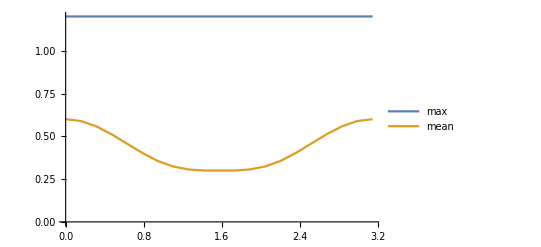

```mathematica
ListLinePlot[{wtmmax,wtmmean},PlotLegends->{"max","mean"}]
```

```mathematica
Dimensions[wtmn[[1]]]
```

{500}

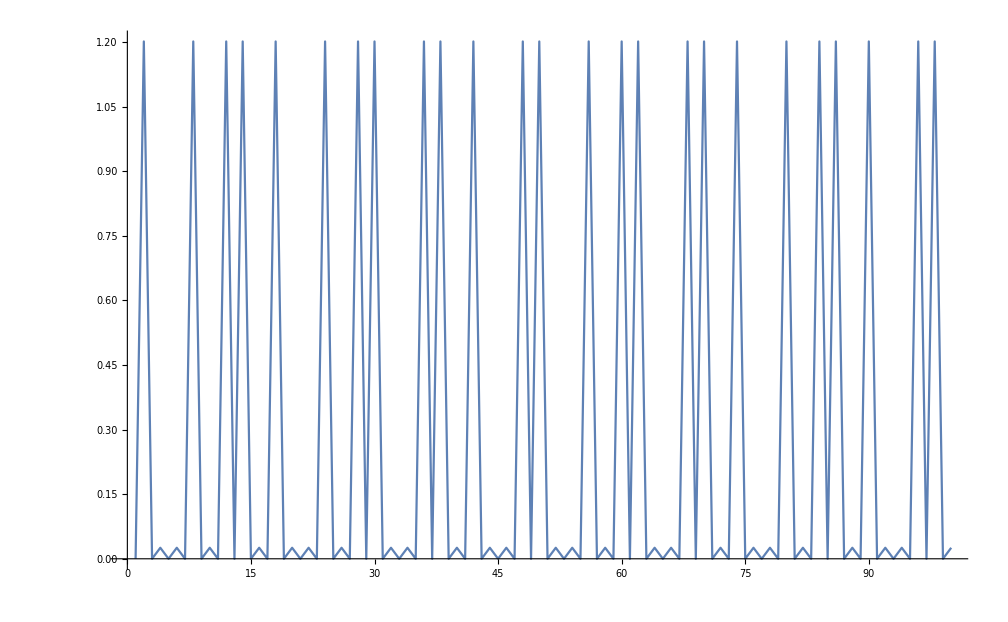

```mathematica
ListLinePlot[Drop[wtmn[[9]],400]]
```

## dt = pi/8 kick*after

#### data

```mathematica
kadata={-0.000000000000000000*10^+00,1.201752073385712993*10^+00,2.147215261966105349*10^+00,2.233645517748440668*10^+00,2.147215261966109789*10^+00,2.233645517748441556*10^+00,2.233645517748428677*10^+00,2.233645517748427789*10^+00,1.404764034988905674*10^+00,1.201752073385705000*10^+00,2.000000000000004885*10^+00,1.201752073385709441*10^+00,2.000000000000004441*10^+00,1.201752073385709441*10^+00,1.404764034988912336*10^+00,2.233645517748437559*10^+00,1.404764034988913668*10^+00,2.233645517748438891*10^+00,2.233645517748438891*10^+00,2.233645517748439779*10^+00,2.233645517748439779*10^+00,2.233645517748441112*10^+00,2.147215261966112454*10^+00,1.201752073385708552*10^+00,-2.434604142899358036*10^-14,1.201752073385708774*10^+00,2.147215261966117339*10^+00,2.233645517748453990*10^+00,2.147215261966120892*10^+00,2.233645517748455767*10^+00,2.233645517748442444*10^+00,2.233645517748439335*10^+00,1.404764034988906118*10^+00,1.201752073385702113*10^+00,2.000000000000013767*10^+00,1.201752073385706110*10^+00,2.000000000000013323*10^+00,1.201752073385705888*10^+00,1.404764034988912114*10^+00,2.233645517748450438*10^+00,2.233645517748450438*10^+00,2.233645517748450438*10^+00,2.147215261966120003*10^+00,1.201752073385704112*10^+00,2.147215261966121780*10^+00,1.201752073385703667*10^+00,-4.677002695569855664*10^-14,1.201752073385704778*10^+00,-4.869208285798757092*10^-14,1.201752073385704334*10^+00,2.147215261966130218*10^+00,2.233645517748467313*10^+00,2.147215261966132438*10^+00,2.233645517748469089*10^+00,2.233645517748457099*10^+00,2.233645517748453990*10^+00,1.404764034988905452*10^+00,1.201752073385697894*10^+00,2.000000000000023093*10^+00,1.201752073385701447*10^+00,2.000000000000023093*10^+00,1.201752073385701447*10^+00,1.404764034988912114*10^+00,2.233645517748465092*10^+00,1.404764034988912780*10^+00,2.233645517748467313*10^+00,2.233645517748466869*10^+00,2.233645517748468645*10^+00,2.233645517748467313*10^+00,2.233645517748468645*10^+00,2.147215261966136879*10^+00,1.201752073385699671*10^+00,-7.303812428698197485*10^-14,1.201752073385700115*10^+00,2.147215261966141320*10^+00,2.233645517748481080*10^+00,2.147215261966144428*10^+00,2.233645517748482856*10^+00,2.233645517748469977*10^+00,2.233645517748467313*10^+00,2.233645517748470866*10^+00,2.233645517748467757*10^+00,1.404764034988905008*10^+00,1.201752073385693453*10^+00,1.404764034988902788*10^+00,1.201752073385693897*10^+00,2.000000000000034195*10^+00,1.201752073385696784*10^+00,1.404764034988909227*10^+00,2.233645517748477083*10^+00,2.233645517748477971*10^+00,2.233645517748478415*10^+00,2.233645517748477083*10^+00,2.233645517748478859*10^+00,2.147215261966147093*10^+00,1.201752073385694342*10^+00,-9.674348041521376108*10^-14,1.201752073385696340*10^+00,2.147215261966153754*10^+00,2.233645517748493958*10^+00,2.147215261966156419*10^+00,2.233645517748494846*10^+00,2.233645517748481968*10^+00,2.233645517748479747*10^+00,1.404764034988901455*10^+00,1.201752073385689012*10^+00,2.000000000000042188*10^+00,1.201752073385693675*10^+00,2.000000000000042188*10^+00,1.201752073385693453*10^+00,1.404764034988909005*10^+00,2.233645517748489961*10^+00,1.404764034988910115*10^+00,2.233645517748492182*10^+00,2.233645517748493070*10^+00,2.233645517748492626*10^+00,2.233645517748492182*10^+00,2.233645517748493514*10^+00,2.147215261966158195*10^+00,1.201752073385691455*10^+00,-1.204488365434459133*10^-13,1.201752073385692121*10^+00,2.147215261966163968*10^+00,2.233645517748508169*10^+00,2.147215261966168409*10^+00,2.233645517748509501*10^+00,2.233645517748495735*10^+00,2.233645517748492626*10^+00,1.404764034988902566*10^+00,1.201752073385685460*10^+00,2.000000000000051514*10^+00,1.201752073385689457*10^+00,2.000000000000051514*10^+00,1.201752073385689457*10^+00,1.404764034988909227*10^+00,2.233645517748503728*10^+00,2.233645517748502840*10^+00,2.233645517748504172*10^+00,2.147215261966168409*10^+00,1.201752073385687236*10^+00,2.147215261966169297*10^+00,1.201752073385686348*10^+00,-1.435135073709154732*10^-13,1.201752073385688790*10^+00,-1.441541926716785074*10^-13,1.201752073385688346*10^+00,2.147215261966176847*10^+00,2.233645517748520160*10^+00,2.147215261966180400*10^+00,2.233645517748522824*10^+00,2.233645517748508613*10^+00,2.233645517748506393*10^+00,1.404764034988901233*10^+00,1.201752073385681463*10^+00,2.000000000000059952*10^+00,1.201752073385685460*10^+00,2.000000000000060396*10^+00,1.201752073385685460*10^+00,1.404764034988909449*10^+00,2.233645517748516163*10^+00,2.233645517748517051*10^+00,2.233645517748516607*10^+00,2.147215261966178623*10^+00,1.201752073385683239*10^+00,2.147215261966180400*10^+00,1.201752073385682351*10^+00,-1.659374928976222764*10^-13,1.201752073385684572*10^+00,2.147215261966186617*10^+00,2.233645517748531706*10^+00,2.233645517748522824*10^+00,2.233645517748522380*10^+00,2.233645517748522824*10^+00,2.233645517748522380*10^+00,1.404764034988906785*10^+00,1.201752073385679687*10^+00,1.404764034988905230*10^+00,1.201752073385680797*10^+00,2.000000000000068834*10^+00,1.201752073385681019*10^+00,2.000000000000068834*10^+00,1.201752073385681685*10^+00,1.404764034988910115*10^+00,2.233645517748529485*10^+00,2.233645517748529929*10^+00,2.233645517748530374*10^+00,2.147215261966190614*10^+00,1.201752073385679909*10^+00,2.147215261966191058*10^+00,1.201752073385678798*10^+00,-1.896428490258556025*10^-13,1.201752073385681019*10^+00,-2.063006668456954513*10^-13,1.201752073385678132*10^+00,2.147215261966206601*10^+00,2.233645517748554798*10^+00,2.147215261966209709*10^+00,2.233645517748556575*10^+00,2.233645517748543696*10^+00,2.233645517748541032*10^+00,2.722912528242654327*10^-14,1.157960598926154105*10^+00,2.054509832576697725*10^+00,2.138929527109509010*10^+00,2.054509832576701278*10^+00,2.138929527109509898*10^+00,2.179919851265774255*10^+00,2.182414474794411419*10^+00,1.429261741750358361*10^+00,1.335218325170752340*10^+00,2.087883932226973105*10^+00,1.335218325170755449*10^+00,2.087883932226972661*10^+00,1.335218325170755893*10^+00,1.429261741750364356*10^+00,2.182414474794420745*10^+00,1.429261741750365911*10^+00,2.182414474794422965*10^+00,2.179919851265784914*10^+00,2.138929527109509010*10^+00,2.179919851265785802*10^+00,2.138929527109509898*10^+00,2.054509832576705719*10^+00,1.157960598926148776*10^+00,-0.000000000000000000*10^+00,1.157960598926148332*10^+00,2.054509832576707939*10^+00,2.138929527109518336*10^+00,2.054509832576711936*10^+00,2.138929527109519668*10^+00,2.179919851265785358*10^+00,2.182414474794425630*10^+00,1.429261741750362358*10^+00,1.335218325170748788*10^+00,2.087883932226983319*10^+00,1.335218325170751230*10^+00,2.087883932226984207*10^+00,1.335218325170752118*10^+00,1.429261741750366133*10^+00,2.182414474794435399*10^+00,2.179919851265794684*10^+00,2.138929527109516116*10^+00,2.054509832576711048*10^+00,1.157960598926144113*10^+00,2.054509832576711936*10^+00,1.157960598926142559*10^+00,-2.466638407937507853*10^-14,1.157960598926144558*10^+00,-2.722912528242705761*10^-14,1.157960598926143447*10^+00,2.054509832576717265*10^+00,2.138929527109531215*10^+00,2.054509832576721262*10^+00,2.138929527109532547*10^+00,2.179919851265798236*10^+00,2.182414474794439840*10^+00,1.429261741750364134*10^+00,1.335218325170744347*10^+00,2.087883932226994421*10^+00,1.335218325170747677*10^+00,2.087883932226993977*10^+00,1.335218325170747455*10^+00,1.429261741750369463*10^+00,2.182414474794450499*10^+00,1.429261741750370351*10^+00,2.182414474794452275*10^+00,2.179919851265807118*10^+00,2.138929527109528550*10^+00,2.179919851265807118*10^+00,2.138929527109530326*10^+00,2.054509832576722594*10^+00,1.157960598926139451*10^+00,-4.741071225646155929*10^-14,1.157960598926140117*10^+00,2.054509832576724371*10^+00,2.138929527109537432*10^+00,2.054509832576727035*10^+00,2.138929527109539208*10^+00,2.179919851265805342*10^+00,2.182414474794448278*10^+00,2.179919851265804898*10^+00,2.182414474794448722*10^+00,1.429261741750365022*10^+00,1.335218325170739462*10^+00,1.429261741750363690*10^+00,1.335218325170740350*10^+00,2.087883932227002859*10^+00,1.335218325170742570*10^+00,1.429261741750369463*10^+00,2.182414474794458492*10^+00,2.179919851265812447*10^+00,2.138929527109532547*10^+00,2.179919851265812003*10^+00,2.138929527109532991*10^+00,2.054509832576727923*10^+00,1.157960598926134344*10^+00,-6.951435513278538766*10^-14,1.157960598926136342*10^+00,2.054509832576730144*10^+00,2.138929527109541429*10^+00,2.054509832576734141*10^+00,2.138929527109542761*10^+00,2.179919851265810671*10^+00,2.182414474794455383*10^+00,1.429261741750363468*10^+00,1.335218325170735243*10^+00,2.087883932227009964*10^+00,1.335218325170739240*10^+00,2.087883932227010408*10^+00,1.335218325170739018*10^+00,1.429261741750368131*10^+00,2.182414474794465153*10^+00,1.429261741750370129*10^+00,2.182414474794468706*10^+00,2.179919851265819108*10^+00,2.138929527109539208*10^+00,2.179919851265820441*10^+00,2.138929527109539652*10^+00,2.054509832576733697*10^+00,1.157960598926131013*10^+00,-8.873491415567594702*10^-14,1.157960598926132789*10^+00,2.054509832576737249*10^+00,2.138929527109548090*10^+00,2.054509832576740358*10^+00,2.138929527109549866*10^+00,2.179919851265818220*10^+00,2.182414474794465598*10^+00,1.429261741750364356*10^+00,1.335218325170731912*10^+00,2.087883932227017958*10^+00,1.335218325170735021*10^+00,2.087883932227017514*10^+00,1.335218325170735909*10^+00,1.429261741750370796*10^+00,2.182414474794478032*10^+00,2.179919851265826214*10^+00,2.138929527109545425*10^+00,2.054509832576739914*10^+00,1.157960598926127904*10^+00,2.054509832576741246*10^+00,1.157960598926126572*10^+00,-1.153233541373416396*10^-13,1.157960598926127682*10^+00,-1.207691791938274431*10^-13,1.157960598926126572*10^+00,2.054509832576749240*10^+00,2.138929527109563633*10^+00,2.054509832576752348*10^+00,2.138929527109564965*10^+00,2.179919851265835540*10^+00,2.182414474794485137*10^+00,1.429261741750369685*10^+00,1.335218325170727693*10^+00,2.087883932227031281*10^+00,1.335218325170730580*10^+00,2.087883932227031281*10^+00,1.335218325170730802*10^+00,1.429261741750375680*10^+00,2.182414474794494907*10^+00,2.179919851265841757*10^+00,2.138929527109560524*10^+00,2.054509832576751460*10^+00,1.157960598926121465*10^+00,2.054509832576751904*10^+00,1.157960598926120133*10^+00,-1.451152206228230713*10^-13,1.157960598926122575*10^+00,2.054509832576757233*10^+00,2.138929527109572959*10^+00,2.179919851265846642*10^+00,2.182414474794500236*10^+00,2.179919851265846642*10^+00,2.182414474794500236*10^+00,1.429261741750375458*10^+00,1.335218325170725473*10^+00,1.429261741750374348*10^+00,1.335218325170725917*10^+00,2.087883932227040606*10^+00,1.335218325170727027*10^+00,2.087883932227041939*10^+00,1.335218325170727471*10^+00,1.429261741750377679*10^+00,2.182414474794509118*10^+00,2.179919851265852415*10^+00,2.138929527109571183*10^+00,2.054509832576760786*10^+00,1.157960598926117690*10^+00,2.054509832576762562*10^+00,1.157960598926116358*10^+00,-1.704222900029636674*10^-13,1.157960598926118134*10^+00,-1.758681150594496980*10^-13,1.157960598926117468*10^+00,2.054509832576769668*10^+00,2.138929527109587170*10^+00,2.054509832576772776*10^+00,2.138929527109588946*10^+00,2.179919851265860409*10^+00,2.182414474794515336*10^+00,-9.610279511444755881*10^-16,1.033390542523311195*10^+00,1.780137992344393405*10^+00,1.885810369113252838*10^+00,1.780137992344395181*10^+00,1.885810369113254170*10^+00,2.035583313486590384*10^+00,2.003163981752199785*10^+00,1.497371078476115391*10^+00,1.599820275635258859*10^+00,2.154482367428334655*10^+00,1.599820275635260192*10^+00,2.154482367428334655*10^+00,1.599820275635261524*10^+00,1.497371078476118056*10^+00,2.003163981752203782*10^+00,1.497371078476119610*10^+00,2.003163981752204670*10^+00,2.035583313486596158*10^+00,1.885810369113249285*10^+00,2.035583313486596158*10^+00,1.885810369113250395*10^+00,1.780137992344396292*10^+00,1.033390542523306088*10^+00,-1.825953107174514661*10^-14,1.033390542523306088*10^+00,1.780137992344398956*10^+00,1.885810369113257945*10^+00,1.780137992344401177*10^+00,1.885810369113258389*10^+00,2.035583313486594825*10^+00,2.003163981752203782*10^+00,1.497371078476115835*10^+00,1.599820275635256861*10^+00,2.154482367428342648*10^+00,1.599820275635258193*10^+00,2.154482367428342648*10^+00,1.599820275635258859*10^+00,1.497371078476119166*10^+00,2.003163981752207778*10^+00,2.035583313486599266*10^+00,1.885810369113252394*10^+00,1.780137992344398956*10^+00,1.033390542523300315*10^+00,1.780137992344400288*10^+00,1.033390542523299205*10^+00,-3.908180334654252474*10^-14,1.033390542523301425*10^+00,-4.260557250073902989*10^-14,1.033390542523300537*10^+00,1.780137992344406728*10^+00,1.885810369113265939*10^+00,1.780137992344408504*10^+00,1.885810369113267493*10^+00,2.035583313486604151*10^+00,2.003163981752212663*10^+00,1.497371078476117612*10^+00,1.599820275635256195*10^+00,2.154482367428353751*10^+00,1.599820275635259303*10^+00,2.154482367428353307*10^+00,1.599820275635259526*10^+00,1.497371078476121387*10^+00,2.003163981752216216*10^+00,1.497371078476121387*10^+00,2.003163981752217548*10^+00,2.035583313486609924*10^+00,1.885810369113261942*10^+00,2.035583313486610368*10^+00,1.885810369113263052*10^+00,1.780137992344408726*10^+00,1.033390542523294320*10^+00,-6.438887272668129066*10^-14,1.033390542523294986*10^+00,1.780137992344412723*10^+00,1.885810369113271490*10^+00,1.780137992344414721*10^+00,1.885810369113272156*10^+00,2.035583313486610813*10^+00,2.003163981752216660*10^+00,2.035583313486610813*10^+00,2.003163981752217992*10^+00,1.497371078476118722*10^+00,1.599820275635255751*10^+00,1.497371078476116946*10^+00,1.599820275635254863*10^+00,2.154482367428363521*10^+00,1.599820275635257083*10^+00,1.497371078476118722*10^+00,2.003163981752220657*10^+00,2.035583313486614809*10^+00,1.885810369113266161*10^+00,2.035583313486615253*10^+00,1.885810369113266605*10^+00,1.780137992344414499*10^+00,1.033390542523287881*10^+00,-8.617217295262386066*10^-14,1.033390542523289435*10^+00,1.780137992344417386*10^+00,1.885810369113275264*10^+00,1.780137992344419606*10^+00,1.885810369113276819*10^+00,2.035583313486614809*10^+00,2.003163981752219769*10^+00,1.497371078476116280*10^+00,1.599820275635253308*10^+00,2.154482367428369738*10^+00,1.599820275635255751*10^+00,2.154482367428370182*10^+00,1.599820275635256639*10^+00,1.497371078476119166*10^+00,2.003163981752224654*10^+00,1.497371078476120054*10^+00,2.003163981752225986*10^+00,2.035583313486620582*10^+00,1.885810369113270824*10^+00,2.035583313486621471*10^+00,1.885810369113271268*10^+00,1.780137992344420050*10^+00,1.033390542523283884*10^+00,-1.053927319755146472*10^-13,1.033390542523284994*10^+00,1.780137992344424047*10^+00,1.885810369113279261*10^+00,1.780137992344425157*10^+00,1.885810369113281482*10^+00,2.035583313486618806*10^+00,2.003163981752223766*10^+00,1.497371078476115613*10^+00,1.599820275635250866*10^+00,2.154482367428377287*10^+00,1.599820275635253530*10^+00,2.154482367428377287*10^+00,1.599820275635253530*10^+00,1.497371078476119388*10^+00,2.003163981752228207*10^+00,2.035583313486623247*10^+00,1.885810369113273932*10^+00,1.780137992344422715*10^+00,1.033390542523279443*10^+00,1.780137992344424047*10^+00,1.033390542523278333*10^+00,-1.268556895510763312*10^-13,1.033390542523279887*10^+00,-1.323015146075621851*10^-13,1.033390542523278999*10^+00,1.780137992344431153*10^+00,1.885810369113289253*10^+00,1.780137992344433151*10^+00,1.885810369113290363*10^+00,2.035583313486629464*10^+00,2.003163981752233536*10^+00,1.497371078476120054*10^+00,1.599820275635251532*10^+00,2.154482367428389278*10^+00,1.599820275635253530*10^+00,2.154482367428389278*10^+00,1.599820275635253752*10^+00,1.497371078476121831*10^+00,2.003163981752236644*10^+00,2.035583313486634793*10^+00,1.885810369113284368*10^+00,1.780137992344432041*10^+00,1.033390542523273226*10^+00,1.780137992344432485*10^+00,1.033390542523272115*10^+00,-1.531237868823611883*10^-13,1.033390542523274558*10^+00,1.780137992344437814*10^+00,1.885810369113295248*10^+00,2.035583313486638790*10^+00,2.003163981752241529*10^+00,2.035583313486639678*10^+00,2.003163981752242861*10^+00,1.497371078476124273*10^+00,1.599820275635251754*10^+00,1.497371078476124495*10^+00,1.599820275635253752*10^+00,2.154482367428399492*10^+00,1.599820275635253974*10^+00,2.154482367428399492*10^+00,1.599820275635254641*10^+00,1.497371078476125605*10^+00,2.003163981752245970*10^+00,2.035583313486642787*10^+00,1.885810369113291696*10^+00,1.780137992344439812*10^+00,1.033390542523268785*10^+00,1.780137992344440701*10^+00,1.033390542523267897*10^+00,-1.755477724090681683*10^-13,1.033390542523269895*10^+00,-1.806732548151726692*10^-13,1.033390542523269007*10^+00,1.780137992344446696*10^+00,1.885810369113305462*10^+00,1.780137992344449804*10^+00,1.885810369113307461*10^+00,2.035583313486649004*10^+00,2.003163981752249523*10^+00,9.610279511444749964*10^-16,8.474263344968472333*10^-01,1.425971808304535626*10^+00,1.548364704965806693*10^+00,1.425971808304536292*10^+00,1.548364704965807359*10^+00,1.845409488735006320*10^+00,1.789764403774479318*10^+00,1.551132257661063996*10^+00,1.783254699214916972*10^+00,2.131149886467653687*10^+00,1.783254699214918970*10^+00,2.131149886467653243*10^+00,1.783254699214918970*10^+00,1.551132257661065772*10^+00,1.789764403774479984*10^+00,1.551132257661065550*10^+00,1.789764403774480872*10^+00,1.845409488735007875*10^+00,1.548364704965802918*10^+00,1.845409488735008763*10^+00,1.548364704965803584*10^+00,1.425971808304534960*10^+00,8.474263344968390177*10^-01,-2.370535612823058401*10^-14,8.474263344968393508*10^-01,1.425971808304536737*10^+00,1.548364704965809358*10^+00,1.425971808304538957*10^+00,1.548364704965809580*10^+00,1.845409488735008541*10^+00,1.789764403774480650*10^+00,1.551132257661061331*10^+00,1.783254699214916306*10^+00,2.131149886467658572*10^+00,1.783254699214917638*10^+00,2.131149886467659016*10^+00,1.783254699214917860*10^+00,1.551132257661062885*10^+00,1.789764403774482204*10^+00,1.845409488735008985*10^+00,1.548364704965803806*10^+00,1.425971808304534738*10^+00,8.474263344968318012*10^-01,1.425971808304535404*10^+00,8.474263344968313572*10^-01,-4.484797105340954235*10^-14,8.474263344968323564*10^-01,-5.061413876027658521*10^-14,8.474263344968320233*10^-01,1.425971808304542288*10^+00,1.548364704965814909*10^+00,1.425971808304544508*10^+00,1.548364704965814909*10^+00,1.845409488735013648*10^+00,1.789764403774486645*10^+00,1.551132257661062663*10^+00,1.783254699214918526*10^+00,2.131149886467668342*10^+00,1.783254699214919636*10^+00,2.131149886467667898*10^+00,1.783254699214919414*10^+00,1.551132257661065328*10^+00,1.789764403774487089*10^+00,1.551132257661064884*10^+00,1.789764403774488200*10^+00,1.845409488735014536*10^+00,1.548364704965811356*10^+00,1.845409488735016090*10^+00,1.548364704965812244*10^+00,1.425971808304544064*10^+00,8.474263344968246958*10^-01,-7.015504043354839662*10^-14,8.474263344968251399*10^-01,1.425971808304544730*10^+00,1.548364704965816907*10^+00,1.425971808304547839*10^+00,1.548364704965817573*10^+00,1.845409488735014314*10^+00,1.789764403774488422*10^+00,1.845409488735014314*10^+00,1.789764403774489088*10^+00,1.551132257661060887*10^+00,1.783254699214916750*10^+00,1.551132257661061331*10^+00,1.783254699214916972*10^+00,2.131149886467674559*10^+00,1.783254699214919414*10^+00,1.551132257661063107*10^+00,1.789764403774488866*10^+00,1.845409488735015424*10^+00,1.548364704965811800*10^+00,1.845409488735016090*10^+00,1.548364704965811800*10^+00,1.425971808304542954*10^+00,8.474263344968167022*10^-01,-9.097731270834654152*10^-14,8.474263344968178124*10^-01,1.425971808304546729*10^+00,1.548364704965818017*10^+00,1.425971808304546729*10^+00,1.548364704965818461*10^+00,1.845409488735014536*10^+00,1.789764403774487533*10^+00,1.551132257661059777*10^+00,1.783254699214916972*10^+00,2.131149886467677668*10^+00,1.783254699214918970*10^+00,2.131149886467677224*10^+00,1.783254699214918304*10^+00,1.551132257661061331*10^+00,1.789764403774487533*10^+00,1.551132257661060887*10^+00,1.789764403774489310*10^+00,1.845409488735015424*10^+00,1.548364704965814465*10^+00,1.845409488735016978*10^+00,1.548364704965814909*10^+00,1.425971808304545618*10^+00,8.474263344968112621*10^-01,-1.082758158289482886*10^-13,8.474263344968119283*10^-01,1.425971808304547173*10^+00,1.548364704965819572*10^+00,1.425971808304550059*10^+00,1.548364704965820238*10^+00,1.845409488735014758*10^+00,1.789764403774487977*10^+00,1.551132257661058667*10^+00,1.783254699214916528*10^+00,2.131149886467681664*10^+00,1.783254699214917638*10^+00,2.131149886467682109*10^+00,1.783254699214917194*10^+00,1.551132257661059777*10^+00,1.789764403774488866*10^+00,1.845409488735016090*10^+00,1.548364704965814909*10^+00,1.425971808304546062*10^+00,8.474263344968047118*10^-01,1.425971808304546951*10^+00,8.474263344968042677*10^-01,-1.271760322014578357*10^-13,8.474263344968059330*10^-01,-1.310201440060360662*10^-13,8.474263344968051559*10^-01,1.425971808304551391*10^+00,1.548364704965824235*10^+00,1.425971808304553168*10^+00,1.548364704965824679*10^+00,1.845409488735019199*10^+00,1.789764403774491974*10^+00,1.551132257661058667*10^+00,1.783254699214916972*10^+00,2.131149886467688326*10^+00,1.783254699214918748*10^+00,2.131149886467688770*10^+00,1.783254699214919414*10^+00,1.551132257661059999*10^+00,1.789764403774492196*10^+00,1.845409488735020087*10^+00,1.548364704965819350*10^+00,1.425971808304549171*10^+00,8.474263344967980505*10^-01,1.425971808304550059*10^+00,8.474263344967971623*10^-01,-1.489593324274013523*10^-13,8.474263344967987166*10^-01,1.425971808304552946*10^+00,1.548364704965826455*10^+00,1.845409488735024528*10^+00,1.789764403774496859*10^+00,1.845409488735023640*10^+00,1.789764403774497303*10^+00,1.551132257661065550*10^+00,1.783254699214921635*10^+00,1.551132257661064884*10^+00,1.783254699214922967*10^+00,2.131149886467695875*10^+00,1.783254699214923411*10^+00,2.131149886467695431*10^+00,1.783254699214923633*10^+00,1.551132257661064884*10^+00,1.789764403774496859*10^+00,1.845409488735024750*10^+00,1.548364704965823124*10^+00,1.425971808304550947*10^+00,8.474263344967916112*10^-01,1.425971808304551613*10^+00,8.474263344967907230*10^-01,-1.685002341006745143*10^-13,8.474263344967923883*10^-01,-1.713833179541082818*10^-13,8.474263344967920553*10^-01,1.425971808304556943*10^+00,1.548364704965831784*10^+00,1.425971808304557609*10^+00,1.548364704965832672*10^+00,1.845409488735027193*10^+00,1.789764403774500190*10^+00,4.805139755722374982*10^-16,6.289791881778419302*10^-01,1.020558494617659129*10^+00,1.277677184678039035*10^+00,1.020558494617658685*10^+00,1.277677184678037925*10^+00,1.681514590162787037*10^+00,1.670219529540810655*10^+00,1.631181954703557091*10^+00,1.878065579073143088*10^+00,2.040087289536599791*10^+00,1.878065579073144420*10^+00,2.040087289536598902*10^+00,1.878065579073144642*10^+00,1.631181954703557979*10^+00,1.670219529540810210*10^+00,1.631181954703557313*10^+00,1.670219529540810877*10^+00,1.681514590162785705*10^+00,1.277677184678033928*10^+00,1.681514590162785705*10^+00,1.277677184678033928*10^+00,1.020558494617653800*10^+00,6.289791881778318272*10^-01,-1.665781781983766837*10^-14,6.289791881778319382*10^-01,1.020558494617653800*10^+00,1.277677184678035927*10^+00,1.020558494617653356*10^+00,1.277677184678035482*10^+00,1.681514590162785039*10^+00,1.670219529540811765*10^+00,1.631181954703555315*10^+00,1.878065579073142866*10^+00,2.040087289536600679*10^+00,1.878065579073144198*10^+00,2.040087289536600679*10^+00,1.878065579073143532*10^+00,1.631181954703554648*10^+00,1.670219529540810655*10^+00,1.681514590162783485*10^+00,1.277677184678029931*10^+00,1.020558494617646916*10^+00,6.289791881778229454*10^-01,1.020558494617646694*10^+00,6.289791881778219462*10^-01,-3.459700624120152507*10^-14,6.289791881778229454*10^-01,-3.619871949310902225*10^-14,6.289791881778229454*10^-01,1.020558494617649137*10^+00,1.277677184678033706*10^+00,1.020558494617648915*10^+00,1.277677184678033928*10^+00,1.681514590162785483*10^+00,1.670219529540814207*10^+00,1.631181954703555537*10^+00,1.878065579073145974*10^+00,2.040087289536606896*10^+00,1.878065579073146196*10^+00,2.040087289536605564*10^+00,1.878065579073145086*10^+00,1.631181954703554648*10^+00,1.670219529540811987*10^+00,1.631181954703554204*10^+00,1.670219529540813541*10^+00,1.681514590162785261*10^+00,1.277677184678028821*10^+00,1.681514590162786593*10^+00,1.277677184678029487*10^+00,1.020558494617642920*10^+00,6.289791881778128424*10^-01,-5.477859321523613719*10^-14,6.289791881778126204*10^-01,1.020558494617642697*10^+00,1.277677184678030597*10^+00,1.020558494617643142*10^+00,1.277677184678030375*10^+00,1.681514590162785483*10^+00,1.670219529540814651*10^+00,1.681514590162785705*10^+00,1.670219529540816206*10^+00,1.631181954703552872*10^+00,1.878065579073145752*10^+00,1.631181954703553538*10^+00,1.878065579073146640*10^+00,2.040087289536610449*10^+00,1.878065579073147306*10^+00,1.631181954703553094*10^+00,1.670219529540815318*10^+00,1.681514590162785705*10^+00,1.277677184678024602*10^+00,1.681514590162786593*10^+00,1.277677184678024602*10^+00,1.020558494617634260*10^+00,6.289791881777998528*10^-01,-7.496018018927102700*10^-14,6.289791881778008520*10^-01,1.020558494617635592*10^+00,1.277677184678026823*10^+00,1.020558494617635148*10^+00,1.277677184678026823*10^+00,1.681514590162786149*10^+00,1.670219529540817760*10^+00,1.631181954703552872*10^+00,1.878065579073147084*10^+00,2.040087289536613557*10^+00,1.878065579073148639*10^+00,2.040087289536611781*10^+00,1.878065579073147973*10^+00,1.631181954703553094*10^+00,1.670219529540817538*10^+00,1.631181954703551540*10^+00,1.670219529540816872*10^+00,1.681514590162785483*10^+00,1.277677184678022826*10^+00,1.681514590162786371*10^+00,1.277677184678022604*10^+00,1.020558494617629819*10^+00,6.289791881777904159*10^-01,-9.289936861063560630*10^-14,6.289791881777910820*10^-01,1.020558494617628931*10^+00,1.277677184678023492*10^+00,1.020558494617628931*10^+00,1.277677184678023270*10^+00,1.681514590162785039*10^+00,1.670219529540819980*10^+00,1.631181954703550652*10^+00,1.878065579073148195*10^+00,2.040087289536616666*10^+00,1.878065579073149083*10^+00,2.040087289536615778*10^+00,1.878065579073148639*10^+00,1.631181954703549764*10^+00,1.670219529540817760*10^+00,1.681514590162783485*10^+00,1.277677184678018163*10^+00,1.020558494617622047*10^+00,6.289791881777814231*10^-01,1.020558494617621825*10^+00,6.289791881777807570*10^-01,-1.101978717312373786*10^-13,6.289791881777818672*10^-01,-1.117995849831449515*10^-13,6.289791881777824223*10^-01,1.020558494617624490*10^+00,1.277677184678023048*10^+00,1.020558494617624490*10^+00,1.277677184678022826*10^+00,1.681514590162787259*10^+00,1.670219529540821757*10^+00,1.631181954703549764*10^+00,1.878065579073149749*10^+00,2.040087289536621551*10^+00,1.878065579073151525*10^+00,2.040087289536621107*10^+00,1.878065579073151081*10^+00,1.631181954703549097*10^+00,1.670219529540819980*10^+00,1.681514590162786593*10^+00,1.277677184678016609*10^+00,1.020558494617618495*10^+00,6.289791881777733185*10^-01,1.020558494617618717*10^+00,6.289791881777717641*10^-01,-1.294184307541284933*10^-13,6.289791881777734295*10^-01,1.020558494617620715*10^+00,1.277677184678020827*10^+00,1.681514590162789924*10^+00,1.670219529540824643*10^+00,1.681514590162789480*10^+00,1.670219529540824421*10^+00,1.631181954703552650*10^+00,1.878065579073154634*10^+00,1.631181954703553538*10^+00,1.878065579073155522*10^+00,2.040087289536627324*10^+00,1.878065579073156188*10^+00,2.040087289536626436*10^+00,1.878065579073155966*10^+00,1.631181954703552650*10^+00,1.670219529540824421*10^+00,1.681514590162789258*10^+00,1.277677184678016609*10^+00,1.020558494617613610*10^+00,6.289791881777652138*10^-01,1.020558494617612499*10^+00,6.289791881777639926*10^-01,-1.454355632732046010*10^-13,6.289791881777649918*10^-01,-1.467169338747306947*10^-13,6.289791881777655469*10^-01,1.020558494617616274*10^+00,1.277677184678020383*10^+00,1.020558494617615830*10^+00,1.277677184678020605*10^+00,1.681514590162791256*10^+00,1.670219529540828196*10^+00,3.203426503814917641*10^-16,4.115261085513801098*10^-01,7.543852518784247563*10^-01,1.142281826296165370*10^+00,7.543852518784237571*10^-01,1.142281826296165148*10^+00,1.695417164753907135*10^+00,1.831149344298637516*10^+00,1.833385954600264212*10^+00,1.913675852755764906*10^+00,1.952678959391820568*10^+00,1.913675852755766016*10^+00,1.952678959391819014*10^+00,1.913675852755764240*10^+00,1.833385954600264212*10^+00,1.831149344298637294*10^+00,1.833385954600265100*10^+00,1.831149344298637960*10^+00,1.695417164753908468*10^+00,1.142281826296160707*10^+00,1.695417164753908246*10^+00,1.142281826296160485*10^+00,7.543852518784173178*10^-01,4.115261085513667871*10^-01,-1.857987372212664163*10^-14,4.115261085513649553*10^-01,7.543852518784154304*10^-01,1.142281826296160041*10^+00,7.543852518784144312*10^-01,1.142281826296159597*10^+00,1.695417164753910688*10^+00,1.831149344298646175*10^+00,1.833385954600269319*10^+00,1.913675852755770901*10^+00,1.952678959391826119*10^+00,1.913675852755771567*10^+00,1.952678959391824343*10^+00,1.913675852755770679*10^+00,1.833385954600269319*10^+00,1.831149344298646398*10^+00,1.695417164753910910*10^+00,1.142281826296154268*10^+00,7.543852518784079919*10^-01,4.115261085513544637*10^-01,7.543852518784069927*10^-01,4.115261085513529649*10^-01,-3.459700624120152507*10^-14,4.115261085513544637*10^-01,-3.331563563967552606*10^-14,4.115261085513557404*10^-01,7.543852518784086580*10^-01,1.142281826296155600*10^+00,7.543852518784084360*10^-01,1.142281826296155600*10^+00,1.695417164753912465*10^+00,1.831149344298651949*10^+00,1.833385954600272427*10^+00,1.913675852755775786*10^+00,1.952678959391828117*10^+00,1.913675852755776008*10^+00,1.952678959391827229*10^+00,1.913675852755774898*10^+00,1.833385954600272871*10^+00,1.831149344298652837*10^+00,1.833385954600273093*10^+00,1.831149344298652615*10^+00,1.695417164753913575*10^+00,1.142281826296150493*10^+00,1.695417164753914907*10^+00,1.142281826296150049*10^+00,7.543852518784005534*10^-01,4.115261085513421957*10^-01,-5.029379610989508703*10^-14,4.115261085513426398*10^-01,7.543852518783997763*10^-01,1.142281826296150271*10^+00,7.543852518783995542*10^-01,1.142281826296150049*10^+00,1.695417164753915129*10^+00,1.831149344298659054*10^+00,1.695417164753916239*10^+00,1.831149344298661052*10^+00,1.833385954600277534*10^+00,1.913675852755779783*10^+00,1.833385954600277090*10^+00,1.913675852755780005*10^+00,1.952678959391832780*10^+00,1.913675852755782225*10^+00,1.833385954600280865*10^+00,1.831149344298664161*10^+00,1.695417164753918016*10^+00,1.142281826296144498*10^+00,1.695417164753919126*10^+00,1.142281826296144498*10^+00,7.543852518783892291*10^-01,4.115261085513254868*10^-01,-7.111606838469292270*10^-14,4.115261085513257644*10^-01,7.543852518783878969*10^-01,1.142281826296144276*10^+00,7.543852518783880079*10^-01,1.142281826296144276*10^+00,1.695417164753919792*10^+00,1.831149344298671267*10^+00,1.833385954600283085*10^+00,1.913675852755785556*10^+00,1.952678959391835445*10^+00,1.913675852755786444*10^+00,1.952678959391834557*10^+00,1.913675852755786222*10^+00,1.833385954600283307*10^+00,1.831149344298671489*10^+00,1.833385954600284418*10^+00,1.831149344298671711*10^+00,1.695417164753920902*10^+00,1.142281826296139613*10^+00,1.695417164753922901*10^+00,1.142281826296139169*10^+00,7.543852518783807914*10^-01,4.115261085513117201*10^-01,-8.777388620453140833*10^-14,4.115261085513123307*10^-01,7.543852518783790151*10^-01,1.142281826296139391*10^+00,7.543852518783791261*10^-01,1.142281826296138947*10^+00,1.695417164753923567*10^+00,1.831149344298680148*10^+00,1.833385954600287526*10^+00,1.913675852755789775*10^+00,1.952678959391838998*10^+00,1.913675852755789997*10^+00,1.952678959391837221*10^+00,1.913675852755788664*10^+00,1.833385954600287304*10^+00,1.831149344298679260*10^+00,1.695417164753924233*10^+00,1.142281826296134728*10^+00,7.543852518783726868*10^-01,4.115261085513010619*10^-01,7.543852518783711325*10^-01,4.115261085512997297*10^-01,-1.041113613739885788*10^-13,4.115261085513010064*10^-01,-1.031503334228440275*10^-13,4.115261085513017836*10^-01,7.543852518783720207*10^-01,1.142281826296134728*10^+00,7.543852518783713546*10^-01,1.142281826296134728*10^+00,1.695417164753925565*10^+00,1.831149344298685477*10^+00,1.833385954600290191*10^+00,1.913675852755794216*10^+00,1.952678959391842772*10^+00,1.913675852755794438*10^+00,1.952678959391841440*10^+00,1.913675852755793994*10^+00,1.833385954600290191*10^+00,1.831149344298685033*10^+00,1.695417164753926009*10^+00,1.142281826296129177*10^+00,7.543852518783648042*10^-01,4.115261085512899597*10^-01,7.543852518783631389*10^-01,4.115261085512888495*10^-01,-1.198081512426829044*10^-13,4.115261085512902373*10^-01,7.543852518783648042*10^-01,1.142281826296130509*10^+00,1.695417164753931338*10^+00,1.831149344298692583*10^+00,1.695417164753930228*10^+00,1.831149344298693249*10^+00,1.833385954600296852*10^+00,1.913675852755801321*10^+00,1.833385954600297740*10^+00,1.913675852755803541*10^+00,1.952678959391847435*10^+00,1.913675852755803319*10^+00,1.952678959391846547*10^+00,1.913675852755801987*10^+00,1.833385954600298184*10^+00,1.831149344298695247*10^+00,1.695417164753931782*10^+00,1.142281826296126068*10^+00,7.543852518783560335*10^-01,4.115261085512773587*10^-01,7.543852518783551453*10^-01,4.115261085512760264*10^-01,-1.383880249648110732*10^-13,4.115261085512770256*10^-01,-1.374269970136665345*10^-13,4.115261085512781358*10^-01,7.543852518783558114*10^-01,1.142281826296127178*10^+00,7.543852518783549232*10^-01,1.142281826296126512*10^+00,1.695417164753932671*10^+00,1.831149344298700576*10^+00,-9.610279511444755881*10^-16,2.237564860125439425*10^-01,6.503468972890409372*10^-01,1.234354502894089878*10^+00,6.503468972890409372*10^-01,1.234354502894089212*10^+00,1.960363399147780683*10^+00,2.293370935222293738*10^+00,2.126570803865091897*10^+00,1.947711412848817547*10^+00,1.945851430401208670*10^+00,1.947711412848818213*10^+00,1.945851430401207338*10^+00,1.947711412848818435*10^+00,2.126570803865092341*10^+00,2.293370935222299067*10^+00,2.126570803865094561*10^+00,2.293370935222299956*10^+00,1.960363399147786456*10^+00,1.234354502894088990*10^+00,1.960363399147788455*10^+00,1.234354502894089656*10^+00,6.503468972890348310*10^-01,2.237564860125243471*10^-01,-2.178330022594160443*10^-14,2.237564860125237365*10^-01,6.503468972890323885*10^-01,1.234354502894089878*10^+00,6.503468972890324995*10^-01,1.234354502894089434*10^+00,1.960363399147792673*10^+00,2.293370935222313278*10^+00,2.126570803865105663*10^+00,1.947711412848827317*10^+00,1.945851430401216220*10^+00,1.947711412848828871*10^+00,1.945851430401214888*10^+00,1.947711412848828427*10^+00,2.126570803865106996*10^+00,2.293370935222316831*10^+00,1.960363399147796892*10^+00,1.234354502894088768*10^+00,6.503468972890267263*10^-01,2.237564860125084432*10^-01,6.503468972890243949*10^-01,2.237564860125063615*10^-01,-4.100385924883153271*10^-14,2.237564860125070831*10^-01,-3.940214599692402922*10^-14,2.237564860125083044*10^-01,6.503468972890246169*10^-01,1.234354502894089212*10^+00,6.503468972890246169*10^-01,1.234354502894089434*10^+00,1.960363399147801777*10^+00,2.293370935222326601*10^+00,2.126570803865115433*10^+00,1.947711412848837309*10^+00,1.945851430401223325*10^+00,1.947711412848838197*10^+00,1.945851430401221993*10^+00,1.947711412848836421*10^+00,2.126570803865115877*10^+00,2.293370935222330154*10^+00,2.126570803865118542*10^+00,2.293370935222331930*10^+00,1.960363399147807328*10^+00,1.234354502894088323*10^+00,1.960363399147807550*10^+00,1.234354502894088768*10^+00,6.503468972890177335*10^-01,2.237564860124886257*10^-01,-6.086510357248471609*10^-14,2.237564860124880983*10^-01,6.503468972890160682*10^-01,1.234354502894088990*10^+00,6.503468972890151800*10^-01,1.234354502894089212*10^+00,1.960363399147812657*10^+00,2.293370935222344364*10^+00,1.960363399147813990*10^+00,2.293370935222348805*10^+00,2.126570803865130976*10^+00,1.947711412848846191*10^+00,2.126570803865130976*10^+00,1.947711412848848411*10^+00,1.945851430401231985*10^+00,1.947711412848849077*10^+00,2.126570803865134085*10^+00,2.293370935222356799*10^+00,1.960363399147822427*10^+00,1.234354502894089212*10^+00,1.960363399147825092*10^+00,1.234354502894089656*10^+00,6.503468972890066313*10^-01,2.237564860124652555*10^-01,-8.425011705033479589*10^-14,2.237564860124659216*10^-01,6.503468972890055211*10^-01,1.234354502894089878*10^+00,6.503468972890040778*10^-01,1.234354502894089878*10^+00,1.960363399147829089*10^+00,2.293370935222371454*10^+00,2.126570803865146519*10^+00,1.947711412848857293*10^+00,1.945851430401239535*10^+00,1.947711412848858181*10^+00,1.945851430401237758*10^+00,1.947711412848857293*10^+00,2.126570803865145631*10^+00,2.293370935222375451*10^+00,2.126570803865148740*10^+00,2.293370935222376783*10^+00,1.960363399147833530*10^+00,1.234354502894088768*10^+00,1.960363399147835972*10^+00,1.234354502894089878*10^+00,6.503468972889985267*10^-01,2.237564860124465205*10^-01,-1.053927319755146472*10^-13,2.237564860124462152*10^-01,6.503468972889955291*10^-01,1.234354502894090100*10^+00,6.503468972889960842*10^-01,1.234354502894090322*10^+00,1.960363399147840413*10^+00,2.293370935222389662*10^+00,2.126570803865159398*10^+00,1.947711412848866841*10^+00,1.945851430401246418*10^+00,1.947711412848867285*10^+00,1.945851430401246196*10^+00,1.947711412848866397*10^+00,2.126570803865160286*10^+00,2.293370935222394102*10^+00,1.960363399147845520*10^+00,1.234354502894089212*10^+00,6.503468972889904220*10^-01,2.237564860124299226*10^-01,6.503468972889879796*10^-01,2.237564860124280908*10^-01,-1.242929483480241439*10^-13,2.237564860124291177*10^-01,-1.226912350961165457*10^-13,2.237564860124310884*10^-01,6.503468972889880906*10^-01,1.234354502894089656*10^+00,6.503468972889876465*10^-01,1.234354502894089212*10^+00,1.960363399147848407*10^+00,2.293370935222402984*10^+00,2.126570803865168280*10^+00,1.947711412848875501*10^+00,1.945851430401252635*10^+00,1.947711412848875945*10^+00,1.945851430401251747*10^+00,1.947711412848874613*10^+00,2.126570803865169612*10^+00,2.293370935222407425*10^+00,1.960363399147852626*10^+00,1.234354502894088323*10^+00,6.503468972889818733*10^-01,2.237564860124151012*10^-01,6.503468972889794308*10^-01,2.237564860124132138*10^-01,-1.412711088182447903*10^-13,2.237564860124137966*10^-01,6.503468972889796529*10^-01,1.234354502894089212*10^+00,1.960363399147859287*10^+00,2.293370935222418527*10^+00,1.960363399147859953*10^+00,2.293370935222420748*10^+00,2.126570803865181603*10^+00,1.947711412848886825*10^+00,2.126570803865182935*10^+00,1.947711412848888379*10^+00,1.945851430401261739*10^+00,1.947711412848888601*10^+00,1.945851430401260629*10^+00,1.947711412848887269*10^+00,2.126570803865185155*10^+00,2.293370935222427409*10^+00,1.960363399147867280*10^+00,1.234354502894089656*10^+00,6.503468972889716593*10^-01,2.237564860123970045*10^-01,6.503468972889701050*10^-01,2.237564860123951171*10^-01,-1.617730384426624152*10^-13,2.237564860123962274*10^-01,-1.595306398899917324*10^-13,2.237564860123978649*10^-01,6.503468972889699939*10^-01,1.234354502894089434*10^+00,6.503468972889703270*10^-01,1.234354502894089434*10^+00,1.960363399147869945*10^+00,2.293370935222436291*10^+00,-3.203426503814917641*10^-16,9.553703179852060523*10^-02,7.714043066395345205*10^-01,1.480710985696888971*10^+00,7.714043066395352977*10^-01,1.480710985696890081*10^+00,2.351891639353484109*10^+00,2.904567875771817853*10^+00,2.501578717774501026*10^+00,1.943473717543606760*10^+00,1.976734985508785236*10^+00,1.943473717543606982*10^+00,1.976734985508783904*10^+00,1.943473717543605872*10^+00,2.501578717774504135*10^+00,2.904567875771828511*10^+00,2.501578717774507243*10^+00,2.904567875771831176*10^+00,2.351891639353493879*10^+00,1.480710985696891191*10^+00,2.351891639353497432*10^+00,1.480710985696891857*10^+00,7.714043066395301906*10^-01,9.553703179849705462*10^-02,-2.498672672975657355*10^-14,9.553703179849623583*10^-02,7.714043066395280812*10^-01,1.480710985696894300*10^+00,7.714043066395276371*10^-01,1.480710985696894744*10^+00,2.351891639353506314*10^+00,2.904567875771854712*10^+00,2.501578717774527227*10^+00,1.943473717543618307*10^+00,1.976734985508796782*10^+00,1.943473717543618307*10^+00,1.976734985508795894*10^+00,1.943473717543617418*10^+00,2.501578717774529892*10^+00,2.904567875771864038*10^+00,2.351891639353514307*10^+00,1.480710985696895854*10^+00,7.714043066395237513*10^-01,9.553703179847740368*10^-02,7.714043066395216419*10^-01,9.553703179847634896*10^-02,-4.580899900455404949*10^-14,9.553703179847561344*10^-02,-4.260557250073902989*10^-14,9.553703179847775062*10^-02,7.714043066395215309*10^-01,1.480710985696898296*10^+00,7.714043066395218640*10^-01,1.480710985696898518*10^+00,2.351891639353524077*10^+00,2.904567875771880026*10^+00,2.501578717774546767*10^+00,1.943473717543627410*10^+00,1.976734985508806330*10^+00,1.943473717543627854*10^+00,1.976734985508804110*10^+00,1.943473717543626300*10^+00,2.501578717774549432*10^+00,2.904567875771889796*10^+00,2.501578717774552985*10^+00,2.904567875771894236*10^+00,2.351891639353534735*10^+00,1.480710985696900739*10^+00,2.351891639353537400*10^+00,1.480710985696901183*10^+00,7.714043066395173120*10^-01,9.553703179845375593*10^-02,-6.727195658011484364*10^-14,9.553703179845357552*10^-02,7.714043066395150916*10^-01,1.480710985696903403*10^+00,7.714043066395160908*10^-01,1.480710985696904070*10^+00,2.351891639353548058*10^+00,2.904567875771916441*10^+00,2.351891639353550278*10^+00,2.904567875771921770*10^+00,2.501578717774576521*10^+00,1.943473717543640067*10^+00,2.501578717774578298*10^+00,1.943473717543641399*10^+00,1.976734985508818987*10^+00,1.943473717543641843*10^+00,2.501578717774584071*10^+00,2.904567875771939089*10^+00,2.351891639353562269*10^+00,1.480710985696906956*10^+00,2.351891639353567598*10^+00,1.480710985696908732*10^+00,7.714043066395079862*10^-01,9.553703179842318316*10^-02,-9.802485101673981689*10^-14,9.553703179842339133*10^-02,7.714043066395064319*10^-01,1.480710985696910509*10^+00,7.714043066395069870*10^-01,1.480710985696910953*10^+00,2.351891639353576924*10^+00,2.904567875771961738*10^+00,2.501578717774603611*10^+00,1.943473717543653390*10^+00,1.976734985508830311*10^+00,1.943473717543653168*10^+00,1.976734985508830089*10^+00,1.943473717543652057*10^+00,2.501578717774606719*10^+00,2.904567875771971508*10^+00,2.501578717774611604*10^+00,2.904567875771975505*10^+00,2.351891639353587138*10^+00,1.480710985696912507*10^+00,2.351891639353591135*10^+00,1.480710985696914062*10^+00,7.714043066395012138*10^-01,9.553703179839889703*10^-02,-1.223708924457350412*10^-13,9.553703179839853621*10^-02,7.714043066394999926*10^-01,1.480710985696916282*10^+00,7.714043066394991044*10^-01,1.480710985696916726*10^+00,2.351891639353601349*10^+00,2.904567875771998153*10^+00,2.501578717774630700*10^+00,1.943473717543665158*10^+00,1.976734985508842080*10^+00,1.943473717543664936*10^+00,1.976734985508841191*10^+00,1.943473717543663826*10^+00,2.501578717774633809*10^+00,2.904567875772008367*10^+00,2.351891639353609342*10^+00,1.480710985696917836*10^+00,7.714043066394957737*10^-01,9.553703179837966242*10^-02,7.714043066394934423*10^-01,9.553703179837789994*10^-02,-1.435135073709154732*10^-13,9.553703179837738646*10^-02,-1.409507661678632858*10^-13,9.553703179837993997*10^-02,7.714043066394934423*10^-01,1.480710985696920501*10^+00,7.714043066394939974*10^-01,1.480710985696920945*10^+00,2.351891639353620000*10^+00,2.904567875772026131*10^+00,2.501578717774651128*10^+00,1.943473717543674040*10^+00,1.976734985508852738*10^+00,1.943473717543674262*10^+00,1.976734985508850073*10^+00,1.943473717543672485*10^+00,2.501578717774653793*10^+00,2.904567875772035901*10^+00,2.351891639353627994*10^+00,1.480710985696921611*10^+00,7.714043066394900006*10^-01,9.553703179836199599*10^-02,7.714043066394880022*10^-01,9.553703179836035841*10^-02,-1.617730384426624152*10^-13,9.553703179835965065*10^-02,7.714043066394864478*10^-01,1.480710985696925164*10^+00,2.351891639353638652*10^+00,2.904567875772051000*10^+00,2.351891639353640873*10^+00,2.904567875772057661*10^+00,2.501578717774672889*10^+00,1.943473717543685142*10^+00,2.501578717774675553*10^+00,1.943473717543686252*10^+00,1.976734985508863174*10^+00,1.943473717543686696*10^+00,1.976734985508862064*10^+00,1.943473717543685142*10^+00,2.501578717774678662*10^+00,2.904567875772070540*10^+00,2.351891639353651975*10^+00,1.480710985696928272*10^+00,7.714043066394808967*10^-01,9.553703179833895887*10^-02,7.714043066394784542*10^-01,9.553703179833732129*10^-02,-1.854783945708956656*10^-13,9.553703179833716863*10^-02,-1.819546254166987881*10^-13,9.553703179834018011*10^-02,7.714043066394796755*10^-01,1.480710985696930493*10^+00,7.714043066394796755*10^-01,1.480710985696930937*10^+00,2.351891639353660857*10^+00,2.904567875772087859*10^+00,-3.203426503814917641*10^-16,2.557510288560964698*10^-02,9.693353596628000446*10^-01,1.739566506464458095*10^+00,9.693353596628013769*10^-01,1.739566506464458984*10^+00,2.782349856410779587*10^+00,3.467571653685185495*10^+00,2.869940897380621081*10^+00,1.976053825354162630*10^+00,1.976121250040000055*10^+00,1.976053825354162852*10^+00,1.976121250039998722*10^+00,1.976053825354161742*10^+00,2.869940897380624634*10^+00,3.467571653685199262*10^+00,2.869940897380629519*10^+00,3.467571653685203703*10^+00,2.782349856410793798*10^+00,1.739566506464462314*10^+00,2.782349856410800459*10^+00,1.739566506464463647*10^+00,9.693353596627967139*10^-01,2.557510288558160344*10^-02,-2.851049588395304715*10^-14,2.557510288558024342*10^-02,9.693353596627953817*10^-01,1.739566506464467199*10^+00,9.693353596627962698*10^-01,1.739566506464467865*10^+00,2.782349856410811562*10^+00,3.467571653685232569*10^+00,2.869940897380656608*10^+00,1.976053825354176174*10^+00,1.976121250040013599*10^+00,1.976053825354175952*10^+00,1.976121250040012267*10^+00,1.976053825354175064*10^+00,2.869940897380660161*10^+00,3.467571653685245892*10^+00,2.782349856410822220*10^+00,1.739566506464470086*10^+00,9.693353596627933833*10^-01,2.557510288555939898*10^-02,9.693353596627901636*10^-01,2.557510288555714037*10^-02,-5.285653731294711029*10^-14,2.557510288555705016*10^-02,-4.965311080913207806*10^-14,2.557510288556030797*10^-02,9.693353596627912738*10^-01,1.739566506464474749*10^+00,9.693353596627922730*10^-01,1.739566506464475193*10^+00,2.782349856410835987*10^+00,3.467571653685269428*10^+00,2.869940897380683698*10^+00,1.976053825354186610*10^+00,1.976121250040024035*10^+00,1.976053825354187055*10^+00,1.976121250040022481*10^+00,1.976053825354185722*10^+00,2.869940897380688138*10^+00,3.467571653685282751*10^+00,2.869940897380693468*10^+00,3.467571653685286304*10^+00,2.782349856410849753*10^+00,1.739566506464478302*10^+00,2.782349856410855526*10^+00,1.739566506464479856*10^+00,9.693353596627881652*10^-01,2.557510288552999542*10^-02,-7.880429199384913130*10^-14,2.557510288553029379*10^-02,9.693353596627869440*10^-01,1.739566506464483409*10^+00,9.693353596627871660*10^-01,1.739566506464484519*10^+00,2.782349856410868405*10^+00,3.467571653685317390*10^+00,2.782349856410872846*10^+00,3.467571653685324051*10^+00,2.869940897380724998*10^+00,1.976053825354202154*10^+00,2.869940897380727662*10^+00,1.976053825354203486*10^+00,1.976121250040040689*10^+00,1.976053825354203486*10^+00,2.869940897380733880*10^+00,3.467571653685346700*10^+00,2.782349856410888833*10^+00,1.739566506464490292*10^+00,2.782349856410894606*10^+00,1.739566506464492068*10^+00,9.693353596627802826*10^-01,2.557510288549547789*10^-02,-1.146826688365786054*10^-13,2.557510288549537381*10^-02,9.693353596627789504*10^-01,1.739566506464495177*10^+00,9.693353596627796165*10^-01,1.739566506464496065*10^+00,2.782349856410908817*10^+00,3.467571653685375566*10^+00,2.869940897380763190*10^+00,1.976053825354216809*10^+00,1.976121250040054456*10^+00,1.976053825354216809*10^+00,1.976121250040052679*10^+00,1.976053825354215476*10^+00,2.869940897380767630*10^+00,3.467571653685391553*10^+00,2.869940897380771183*10^+00,3.467571653685394661*10^+00,2.782349856410924360*10^+00,1.739566506464499618*10^+00,2.782349856410928801*10^+00,1.739566506464500950*10^+00,9.693353596627751756*10^-01,2.557510288546582106*10^-02,-1.431931647205339182*10^-13,2.557510288546567881*10^-02,9.693353596627741764*10^-01,1.739566506464504947*10^+00,9.693353596627747315*10^-01,1.739566506464505835*10^+00,2.782349856410941236*10^+00,3.467571653685423971*10^+00,2.869940897380799605*10^+00,1.976053825354230575*10^+00,1.976121250040067556*10^+00,1.976053825354230575*10^+00,1.976121250040066446*10^+00,1.976053825354229687*10^+00,2.869940897380803158*10^+00,3.467571653685437738*10^+00,2.782349856410952782*10^+00,1.739566506464508278*10^+00,9.693353596627714008*10^-01,2.557510288544410232*10^-02,9.693353596627698465*10^-01,2.557510288544133717*10^-02,-1.675392061495299251*10^-13,2.557510288544078900*10^-02,-1.646561222960961575*10^-13,2.557510288544383864*10^-02,9.693353596627690694*10^-01,1.739566506464512052*10^+00,9.693353596627698465*10^-01,1.739566506464512941*10^+00,2.782349856410965216*10^+00,3.467571653685459943*10^+00,2.869940897380826694*10^+00,1.976053825354240789*10^+00,1.976121250040078436*10^+00,1.976053825354241233*10^+00,1.976121250040077326*10^+00,1.976053825354240123*10^+00,2.869940897380831579*10^+00,3.467571653685473709*10^+00,2.782349856410975431*10^+00,1.739566506464515605*10^+00,9.693353596627669599*10^-01,2.557510288542293175*10^-02,9.693353596627640734*10^-01,2.557510288541986823*10^-02,-1.899631916762371323*10^-13,2.557510288541952823*10^-02,9.693353596627631852*10^-01,1.739566506464519602*10^+00,2.782349856410989641*10^+00,3.467571653685495470*10^+00,2.782349856410993194*10^+00,3.467571653685502131*10^+00,2.869940897380858225*10^+00,1.976053825354253224*10^+00,2.869940897380860001*10^+00,1.976053825354254112*10^+00,1.976121250040091759*10^+00,1.976053825354254556*10^+00,1.976121250040090871*10^+00,1.976053825354253446*10^+00,2.869940897380864442*10^+00,3.467571653685520339*10^+00,2.782349856411006961*10^+00,1.739566506464524487*10^+00,9.693353596627578561*10^-01,2.557510288539530802*10^-02,9.693353596627558577*10^-01,2.557510288539294532*10^-02,-2.171923169586677650*10^-13,2.557510288539188714*10^-02,-2.133482051540893073*10^-13,2.557510288539460719*10^-02,9.693353596627560798*10^-01,1.739566506464528484*10^+00,9.693353596627567459*10^-01,1.739566506464529372*10^+00,2.782349856411021172*10^+00,3.467571653685542099*10^+00,-9.610279511444755881*10^-16,2.159872206107876715*10^-04,1.137322521314893642*10^+00,1.930339065416589728*10^+00,1.137322521314894974*10^+00,1.930339065416590616*10^+00,3.088959709722918667*10^+00,3.859948193968358865*10^+00,3.114476558150617969*10^+00,1.998254245944465879*10^+00,1.998254503344109256*10^+00,1.998254245944466323*10^+00,1.998254503344108146*10^+00,1.998254245944464547*10^+00,3.114476558150622409*10^+00,3.859948193968374852*10^+00,3.114476558150627294*10^+00,3.859948193968379293*10^+00,3.088959709722936431*10^+00,1.930339065416595057*10^+00,3.088959709722941760*10^+00,1.930339065416596611*10^+00,1.137322521314891199*10^+00,2.159872205798792088*10^-04,-3.203426503814953337*10^-14,2.159872205787581980*10^-04,1.137322521314889423*10^+00,1.930339065416601496*10^+00,1.137322521314890755*10^+00,1.930339065416602384*10^+00,3.088959709722957747*10^+00,3.859948193968413044*10^+00,3.114476558150657937*10^+00,1.998254245944479202*10^+00,1.998254503344122579*10^+00,1.998254245944478757*10^+00,1.998254503344121469*10^+00,1.998254245944477869*10^+00,3.114476558150662377*10^+00,3.859948193968428143*10^+00,3.088959709722968849*10^+00,1.930339065416605493*10^+00,1.137322521314888535*10^+00,2.159872205571383122*10^-04,1.137322521314886759*10^+00,2.159872205539353622*10^-04,-5.734133441828816676*10^-14,2.159872205532947613*10^-04,-5.381756526409161743*10^-14,2.159872205560172743*10^-04,1.137322521314886092*10^+00,1.930339065416609712*10^+00,1.137322521314887203*10^+00,1.930339065416610378*10^+00,3.088959709722983060*10^+00,3.859948193968452124*10^+00,3.114476558150686802*10^+00,1.998254245944488527*10^+00,1.998254503344132349*10^+00,1.998254245944488749*10^+00,1.998254503344130573*10^+00,1.998254245944487639*10^+00,3.114476558150689911*10^+00,3.859948193968466335*10^+00,3.114476558150695240*10^+00,3.859948193968473440*10^+00,3.088959709723000380*10^+00,1.930339065416614597*10^+00,3.088959709723007041*10^+00,1.930339065416616595*10^+00,1.137322521314883650*10^+00,2.159872205260697129*10^-04,-8.425011705033479589*10^-14,2.159872205260697129*10^-04,1.137322521314882096*10^+00,1.930339065416620592*10^+00,1.137322521314882984*10^+00,1.930339065416621924*10^+00,3.088959709723020364*10^+00,3.859948193968504970*10^+00,3.088959709723025693*10^+00,3.859948193968513852*10^+00,3.114476558150731655*10^+00,1.998254245944503404*10^+00,3.114476558150733432*10^+00,1.998254245944504515*10^+00,1.998254503344148114*10^+00,1.998254245944504515*10^+00,3.114476558150741425*10^+00,3.859948193968538721*10^+00,3.088959709723044789*10^+00,1.930339065416629030*10^+00,3.088959709723052338*10^+00,1.930339065416630806*10^+00,1.137322521314877655*10^+00,2.159872204873140389*10^-04,-1.233319203968796052*10^-13,2.159872204869937656*10^-04,1.137322521314876766*10^+00,1.930339065416635025*10^+00,1.137322521314878099*10^+00,1.930339065416636135*10^+00,3.088959709723066549*10^+00,3.859948193968573804*10^+00,3.114476558150771623*10^+00,1.998254245944517393*10^+00,1.998254503344160993*10^+00,1.998254245944517393*10^+00,1.998254503344159438*10^+00,1.998254245944516061*10^+00,3.114476558150773844*10^+00,3.859948193968587571*10^+00,3.114476558150780505*10^+00,3.859948193968592900*10^+00,3.088959709723082092*10^+00,1.930339065416639910*10^+00,3.088959709723088753*10^+00,1.930339065416641908*10^+00,1.137322521314874102*10^+00,2.159872204567259038*10^-04,-1.537644721831242478*10^-13,2.159872204546439917*10^-04,1.137322521314872770*10^+00,1.930339065416646349*10^+00,1.137322521314874102*10^+00,1.930339065416647237*10^+00,3.088959709723103408*10^+00,3.859948193968625318*10^+00,3.114476558150810259*10^+00,1.998254245944530272*10^+00,1.998254503344173649*10^+00,1.998254245944530272*10^+00,1.998254503344172317*10^+00,1.998254245944529162*10^+00,3.114476558150813812*10^+00,3.859948193968641306*10^+00,3.088959709723115399*10^+00,1.930339065416650346*10^+00,1.137322521314871215*10^+00,2.159872204323835050*10^-04,1.137322521314868773*10^+00,2.159872204299813196*10^-04,-1.806732548151726692*10^-13,2.159872204287001179*10^-04,-1.774698283113573719*10^-13,2.159872204327038326*10^-04,1.137322521314869439*10^+00,1.930339065416654787*10^+00,1.137322521314870105*10^+00,1.930339065416655897*10^+00,3.088959709723130942*10^+00,3.859948193968666175*10^+00,3.114476558150840013*10^+00,1.998254245944540264*10^+00,1.998254503344183419*10^+00,1.998254245944540042*10^+00,1.998254503344181643*10^+00,1.998254245944538932*10^+00,3.114476558150842678*10^+00,3.859948193968679497*10^+00,3.088959709723142488*10^+00,1.930339065416659006*10^+00,1.137322521314867441*10^+00,2.159872204106034826*10^-04,1.137322521314865442*10^+00,2.159872204075606963*10^-04,-2.024565550411169936*10^-13,2.159872204065997950*10^-04,1.137322521314864332*10^+00,1.930339065416664557*10^+00,3.088959709723158920*10^+00,3.859948193968706143*10^+00,3.088959709723163805*10^+00,3.859948193968714136*10^+00,3.114476558150873320*10^+00,1.998254245944552032*10^+00,3.114476558150875096*10^+00,1.998254245944552698*10^+00,1.998254503344196742*10^+00,1.998254245944553364*10^+00,1.998254503344195410*10^+00,1.998254245944552032*10^+00,3.114476558150878205*10^+00,3.859948193968735008*10^+00,3.088959709723179792*10^+00,1.930339065416670330*10^+00,1.137322521314860335*10^+00,2.159872203796950199*10^-04,1.137322521314858337*10^+00,2.159872203764920970*10^-04,-2.348111627296525816*10^-13,2.159872203758514961*10^-04,-2.306467082746924680*10^-13,2.159872203798552108*10^-04,1.137322521314857671*10^+00,1.930339065416674549*10^+00,1.137322521314858781*10^+00,1.930339065416675881*10^+00,3.088959709723194447*10^+00,3.859948193968758545*10^+00,-0.000000000000000000*10^+00,4.805139755722374982*10^-16,1.201752073385712105*10^+00,2.000000000000001776*10^+00,1.201752073385711217*10^+00,2.000000000000003553*10^+00,3.201752073385722319*10^+00,4.000000000000014211*10^+00,3.201752073385725872*10^+00,2.000000000000005329*10^+00,2.000000000000005329*10^+00,2.000000000000005329*10^+00,2.000000000000004441*10^+00,2.000000000000003553*10^+00,3.201752073385729425*10^+00,4.000000000000030198*10^+00,3.201752073385732533*10^+00,4.000000000000034639*10^+00,3.201752073385735198*10^+00,2.000000000000007105*10^+00,3.201752073385742303*10^+00,2.000000000000009326*10^+00,1.201752073385707220*10^+00,-3.011220913586054433*10^-14,-3.075289443662354067*10^-14,-3.107323708700503885*10^-14,1.201752073385707220*10^+00,2.000000000000014211*10^+00,1.201752073385706332*10^+00,2.000000000000015099*10^+00,3.201752073385760067*10^+00,4.000000000000069278*10^+00,3.201752073385764064*10^+00,2.000000000000017319*10^+00,2.000000000000017319*10^+00,2.000000000000017319*10^+00,2.000000000000015987*10^+00,2.000000000000015987*10^+00,3.201752073385768060*10^+00,4.000000000000085265*10^+00,3.201752073385770281*10^+00,2.000000000000018652*10^+00,1.201752073385703223*10^+00,-5.445825056485463271*10^-14,1.201752073385703445*10^+00,-5.702099176790666227*10^-14,-5.670064911752515779*10^-14,-5.734133441828816676*10^-14,-5.381756526409161743*10^-14,-5.381756526409161743*10^-14,1.201752073385703223*10^+00,2.000000000000023093*10^+00,1.201752073385702335*10^+00,2.000000000000023981*10^+00,3.201752073385788488*10^+00,4.000000000000111022*10^+00,3.201752073385791597*10^+00,2.000000000000026645*10^+00,2.000000000000026645*10^+00,2.000000000000026645*10^+00,2.000000000000024869*10^+00,2.000000000000024869*10^+00,3.201752073385796926*10^+00,4.000000000000125233*10^+00,3.201752073385800035*10^+00,4.000000000000131450*10^+00,3.201752073385802255*10^+00,2.000000000000028422*10^+00,3.201752073385808917*10^+00,2.000000000000030642*10^+00,1.201752073385698116*10^+00,-8.489080235109781748*10^-14,-8.553148765186083907*10^-14,-8.521114500147933459*10^-14,1.201752073385698116*10^+00,2.000000000000035083*10^+00,1.201752073385697672*10^+00,2.000000000000036415*10^+00,3.201752073385827124*10^+00,4.000000000000166089*10^+00,3.201752073385833341*10^+00,4.000000000000175859*10^+00,3.201752073385837782*10^+00,2.000000000000040856*10^+00,3.201752073385841335*10^+00,2.000000000000041744*10^+00,2.000000000000041744*10^+00,2.000000000000041744*10^+00,3.201752073385851105*10^+00,4.000000000000203393*10^+00,3.201752073385851105*10^+00,2.000000000000044409*10^+00,3.201752073385859099*10^+00,2.000000000000046185*10^+00,1.201752073385691677*10^+00,-1.255743189495502375*10^-13,-1.258946615999317420*10^-13,-1.262150042503132717*10^-13,1.201752073385691011*10^+00,2.000000000000050626*10^+00,1.201752073385690345*10^+00,2.000000000000051514*10^+00,3.201752073385875974*10^+00,4.000000000000237144*10^+00,3.201752073385880859*10^+00,2.000000000000054179*10^+00,2.000000000000054179*10^+00,2.000000000000054179*10^+00,2.000000000000052847*10^+00,2.000000000000053291*10^+00,3.201752073385885300*10^+00,4.000000000000254019*10^+00,3.201752073385888409*10^+00,4.000000000000257572*10^+00,3.201752073385890185*10^+00,2.000000000000056399*10^+00,3.201752073385896846*10^+00,2.000000000000058176*10^+00,1.201752073385686570*10^+00,-1.572882413373210243*10^-13,-1.572882413373210243*10^-13,-1.572882413373210243*10^-13,1.201752073385686348*10^+00,2.000000000000063061*10^+00,1.201752073385685460*10^+00,2.000000000000064393*10^+00,3.201752073385913722*10^+00,4.000000000000293987*10^+00,3.201752073385919939*10^+00,2.000000000000066169*10^+00,2.000000000000066613*10^+00,2.000000000000066613*10^+00,2.000000000000064837*10^+00,2.000000000000064837*10^+00,3.201752073385923936*10^+00,4.000000000000309086*10^+00,3.201752073385925268*10^+00,2.000000000000067057*10^+00,1.201752073385682795*10^+00,-1.803529121647911394*10^-13,1.201752073385682795*10^+00,-1.829156533678434025*10^-13,-1.829156533678434025*10^-13,-1.835563386686064620*10^-13,-1.800325695144096097*10^-13,-1.806732548151726692*10^-13,1.201752073385682351*10^+00,2.000000000000071942*10^+00,1.201752073385681907*10^+00,2.000000000000072831*10^+00,3.201752073385942143*10^+00,4.000000000000333955*10^+00,3.201752073385947917*10^+00,2.000000000000075051*10^+00,2.000000000000075051*10^+00,2.000000000000075495*10^+00,2.000000000000073719*10^+00,2.000000000000073719*10^+00,3.201752073385952357*10^+00,4.000000000000349054*10^+00,3.201752073385951913*10^+00,2.000000000000076383*10^+00,1.201752073385678798*10^+00,-2.027768976914985486*10^-13,1.201752073385678798*10^+00,-2.059803241953139216*10^-13,-2.063006668456954513*10^-13,-2.069413521464585360*10^-13,1.201752073385678132*10^+00,2.000000000000081712*10^+00,3.201752073385970121*10^+00,4.000000000000375699*10^+00,3.201752073385977226*10^+00,4.000000000000385469*10^+00,3.201752073385982111*10^+00,2.000000000000086153*10^+00,3.201752073385986996*10^+00,2.000000000000087041*10^+00,2.000000000000087486*10^+00,2.000000000000087486*10^+00,2.000000000000085709*10^+00,2.000000000000085709*10^+00,3.201752073385990105*10^+00,4.000000000000403233*10^+00,3.201752073385990993*10^+00,2.000000000000087930*10^+00,1.201752073385673913*10^+00,-2.341704774288894717*10^-13,1.201752073385673913*10^+00,-2.370535612823234159*10^-13,-2.370535612823234159*10^-13,-2.373739039327049709*10^-13,-2.341704774288894717*10^-13,-2.341704774288894717*10^-13,1.201752073385673469*10^+00,2.000000000000092371*10^+00,1.201752073385672803*10^+00,2.000000000000093703*10^+00,3.201752073386008757*10^+00,4.000000000000428990*10^+00,-3.203426503814917641*10^-16,2.159872206103072073*10^-04,1.137322521314893198*10^+00,1.930339065416589284*10^+00,1.137322521314894086*10^+00,1.930339065416590394*10^+00,3.088959709722918667*10^+00,3.859948193968356644*10^+00,3.114476558150616192*10^+00,1.998254245944465435*10^+00,1.998254503344108812*10^+00,1.998254245944465657*10^+00,1.998254503344107480*10^+00,1.998254245944464103*10^+00,3.114476558150620189*10^+00,3.859948193968371299*10^+00,3.114476558150623742*10^+00,3.859948193968375296*10^+00,3.088959709722934655*10^+00,1.930339065416594613*10^+00,3.088959709722940872*10^+00,1.930339065416596611*10^+00,1.137322521314892754*10^+00,2.159872205835626231*10^-04,-2.819015323357155213*10^-14,2.159872205821212847*10^-04,1.137322521314891421*10^+00,1.930339065416601052*10^+00,1.137322521314892310*10^+00,1.930339065416602384*10^+00,3.088959709722954639*10^+00,3.859948193968408159*10^+00,3.114476558150653940*10^+00,1.998254245944476981*10^+00,1.998254503344120359*10^+00,1.998254245944477203*10^+00,1.998254503344119470*10^+00,1.998254245944475649*10^+00,3.114476558150655716*10^+00,3.859948193968421482*10^+00,3.088959709722965741*10^+00,1.930339065416604605*10^+00,1.137322521314890977*10^+00,2.159872205633840486*10^-04,1.137322521314888979*10^+00,2.159872205611419727*10^-04,-5.029379610989508703*10^-14,2.159872205611419727*10^-04,-4.677002695569855664*10^-14,2.159872205645050594*10^-04,1.137322521314888313*10^+00,1.930339065416609046*10^+00,1.137322521314890089*10^+00,1.930339065416609934*10^+00,3.088959709722979952*10^+00,3.859948193968442798*10^+00,3.114476558150678365*10^+00,1.998254245944485419*10^+00,1.998254503344128352*10^+00,1.998254245944485197*10^+00,1.998254503344127464*10^+00,1.998254245944484087*10^+00,3.114476558150680585*10^+00,3.859948193968457453*10^+00,3.114476558150684582*10^+00,3.859948193968462338*10^+00,3.088959709722995051*10^+00,1.930339065416613931*10^+00,3.088959709723002600*10^+00,1.930339065416616151*10^+00,1.137322521314887647*10^+00,2.159872205359988364*10^-04,-7.528052283965253148*10^-14,2.159872205358386997*10^-04,1.137322521314886092*10^+00,1.930339065416620814*10^+00,1.137322521314887647*10^+00,1.930339065416621924*10^+00,3.088959709723015923*10^+00,3.859948193968495644*10^+00,3.088959709723020808*10^+00,3.859948193968503194*10^+00,3.114476558150720553*10^+00,1.998254245944499186*10^+00,3.114476558150721885*10^+00,1.998254245944499852*10^+00,1.998254503344143229*10^+00,1.998254245944499630*10^+00,3.114476558150730323*10^+00,3.859948193968528507*10^+00,3.088959709723039460*10^+00,1.930339065416629030*10^+00,3.088959709723046565*10^+00,1.930339065416631250*10^+00,1.137322521314883428*10^+00,2.159872205006062762*10^-04,-1.098775290808558615*10^-13,2.159872204994852654*10^-04,1.137322521314882096*10^+00,1.930339065416635691*10^+00,1.137322521314883206*10^+00,1.930339065416636579*10^+00,3.088959709723062552*10^+00,3.859948193968560037*10^+00,3.114476558150758745*10^+00,1.998254245944511842*10^+00,1.998254503344155442*10^+00,1.998254245944511620*10^+00,1.998254503344154109*10^+00,1.998254245944510732*10^+00,3.114476558150761409*10^+00,3.859948193968574248*10^+00,3.114476558150765850*10^+00,3.859948193968578245*10^+00,3.088959709723076319*10^+00,1.930339065416640576*10^+00,3.088959709723083424*10^+00,1.930339065416642352*10^+00,1.137322521314881207*10^+00,2.159872204729008178*10^-04,-1.380676823144295435*10^-13,2.159872204733812278*10^-04,1.137322521314880097*10^+00,1.930339065416647015*10^+00,1.137322521314881207*10^+00,1.930339065416648126*10^+00,3.088959709723096303*10^+00,3.859948193968611108*10^+00,3.114476558150794272*10^+00,1.998254245944523610*10^+00,1.998254503344166988*10^+00,1.998254245944523610*10^+00,1.998254503344165434*10^+00,1.998254245944522278*10^+00,3.114476558150796937*10^+00,3.859948193968625318*10^+00,3.088959709723108737*10^+00,1.930339065416651012*10^+00,1.137322521314879875*10^+00,2.159872204532026804*10^-04,1.137322521314878099*10^+00,2.159872204503200308*10^-04,-1.598509825403732621*10^-13,2.159872204498395666*10^-04,-1.560068707357949306*10^-13,2.159872204540033908*10^-04,1.137322521314877211*10^+00,1.930339065416655009*10^+00,1.137322521314878321*10^+00,1.930339065416656341*10^+00,3.088959709723119840*10^+00,3.859948193968646635*10^+00,3.114476558150819141*10^+00,1.998254245944531604*10^+00,1.998254503344175426*10^+00,1.998254245944531604*10^+00,1.998254503344173871*10^+00,1.998254245944530050*10^+00,3.114476558150822250*10^+00,3.859948193968659069*10^+00,3.088959709723132274*10^+00,1.930339065416659006*10^+00,1.137322521314877433*10^+00,2.159872204335045430*10^-04,1.137322521314875656*10^+00,2.159872204320632317*10^-04,-1.784308562625019358*10^-13,2.159872204304617296*10^-04,1.137322521314874324*10^+00,1.930339065416664557*10^+00,3.088959709723146929*10^+00,3.859948193968683494*10^+00,3.088959709723153590*10^+00,3.859948193968693264*10^+00,3.114476558150850671*10^+00,1.998254245944542484*10^+00,3.114476558150852004*10^+00,1.998254245944543595*10^+00,1.998254503344187416*10^+00,1.998254245944543595*10^+00,1.998254503344185862*10^+00,1.998254245944542262*10^+00,3.114476558150856000*10^+00,3.859948193968711472*10^+00,3.088959709723168245*10^+00,1.930339065416670552*10^+00,1.137322521314870993*10^+00,2.159872204054787842*10^-04,1.137322521314869217*10^+00,2.159872204033968721*10^-04,-2.082227227479846802*10^-13,2.159872204033968721*10^-04,-2.043786109434062225*10^-13,2.159872204062795217*10^-04,1.137322521314867885*10^+00,1.930339065416674771*10^+00,1.137322521314868995*10^+00,1.930339065416675659*10^+00,3.088959709723181568*10^+00,3.859948193968733676*10^+00,9.610279511444749964*10^-16,2.557510288561191947*10^-02,9.693353596627998225*10^-01,1.739566506464457429*10^+00,9.693353596628007107*10^-01,1.739566506464458540*10^+00,2.782349856410776923*10^+00,3.467571653685181499*10^+00,2.869940897380615752*10^+00,1.976053825354161297*10^+00,1.976121250039998500*10^+00,1.976053825354161297*10^+00,1.976121250039997168*10^+00,1.976053825354159521*10^+00,2.869940897380617972*10^+00,3.467571653685190824*10^+00,2.869940897380622413*10^+00,3.467571653685196154*10^+00,2.782349856410789801*10^+00,1.739566506464461426*10^+00,2.782349856410796018*10^+00,1.739566506464463647*10^+00,9.693353596628002666*10^-01,2.557510288558892050*10^-02,-2.082227227479711307*10^-14,2.557510288558922582*10^-02,9.693353596627982682*10^-01,1.739566506464467199*10^+00,9.693353596627991564*10^-01,1.739566506464468088*10^+00,2.782349856410808453*10^+00,3.467571653685223687*10^+00,2.869940897380647726*10^+00,1.976053825354172178*10^+00,1.976121250040010269*10^+00,1.976053825354172844*10^+00,1.976121250040008714*10^+00,1.976053825354171289*10^+00,2.869940897380648615*10^+00,3.467571653685235233*10^+00,2.782349856410817335*10^+00,1.739566506464470752*10^+00,9.693353596627980462*10^-01,2.557510288557252390*10^-02,9.693353596627962698*10^-01,2.557510288557153511*10^-02,-3.844111804577952208*10^-14,2.557510288557143102*10^-02,-3.427666359082002689*10^-14,2.557510288557562905*10^-02,9.693353596627958257*10^-01,1.739566506464473861*10^+00,9.693353596627964919*10^-01,1.739566506464474749*10^+00,2.782349856410825772*10^+00,3.467571653685251665*10^+00,2.869940897380665934*10^+00,1.976053825354180393*10^+00,1.976121250040018262*10^+00,1.976053825354180393*10^+00,1.976121250040016264*10^+00,1.976053825354178617*10^+00,2.869940897380667266*10^+00,3.467571653685261879*10^+00,2.869940897380672595*10^+00,3.467571653685264987*10^+00,2.782349856410839095*10^+00,1.739566506464478080*10^+00,2.782349856410844424*10^+00,1.739566506464480078*10^+00,9.693353596627957147*10^-01,2.557510288555449318*10^-02,-5.477859321523613719*10^-14,2.557510288555449318*10^-02,9.693353596627947155*10^-01,1.739566506464483409*10^+00,9.693353596627956037*10^-01,1.739566506464484519*10^+00,2.782349856410854194*10^+00,3.467571653685290745*10^+00,2.782349856410860411*10^+00,3.467571653685299626*10^+00,2.869940897380701461*10^+00,1.976053825354193050*10^+00,2.869940897380704570*10^+00,1.976053825354193938*10^+00,1.976121250040031585*10^+00,1.976053825354194160*10^+00,2.869940897380709011*10^+00,3.467571653685320054*10^+00,2.782349856410874622*10^+00,1.739566506464490292*10^+00,2.782349856410882172*10^+00,1.739566506464492734*10^+00,9.693353596627917179*10^-01,2.557510288552387184*10^-02,-8.553148765186083907*10^-14,2.557510288552397593*10^-02,9.693353596627903856*10^-01,1.739566506464496065*10^+00,9.693353596627911628*10^-01,1.739566506464497397*10^+00,2.782349856410894606*10^+00,3.467571653685346700*10^+00,2.869940897380733436*10^+00,1.976053825354205928*10^+00,1.976121250040043797*10^+00,1.976053825354205928*10^+00,1.976121250040042243*10^+00,1.976053825354204374*10^+00,2.869940897380736544*10^+00,3.467571653685358246*10^+00,2.869940897380739209*10^+00,3.467571653685361799*10^+00,2.782349856410906597*10^+00,1.739566506464500728*10^+00,2.782349856410912814*10^+00,1.739566506464502726*10^+00,9.693353596627900526*10^-01,2.557510288550289210*10^-02,-1.060334172762776688*10^-13,2.557510288550261801*10^-02,9.693353596627887203*10^-01,1.739566506464506501*10^+00,9.693353596627898305*10^-01,1.739566506464507167*10^+00,2.782349856410925248*10^+00,3.467571653685388888*10^+00,2.869940897380765410*10^+00,1.976053825354217253*10^+00,1.976121250040055344*10^+00,1.976053825354217253*10^+00,1.976121250040053567*10^+00,1.976053825354215920*10^+00,2.869940897380765854*10^+00,3.467571653685401767*10^+00,2.782349856410933242*10^+00,1.739566506464509832*10^+00,9.693353596627880542*10^-01,2.557510288548479199*10^-02,9.693353596627864999*10^-01,2.557510288548424382*10^-02,-1.252539762991687331*10^-13,2.557510288548454913*10^-02,-1.214098644945905025*10^-13,2.557510288548751898*10^-02,9.693353596627867219*10^-01,1.739566506464512941*10^+00,9.693353596627871660*10^-01,1.739566506464513829*10^+00,2.782349856410944788*10^+00,3.467571653685418642*10^+00,2.869940897380785838*10^+00,1.976053825354225690*10^+00,1.976121250040063559*10^+00,1.976053825354225690*10^+00,1.976121250040062449*10^+00,1.976053825354224358*10^+00,2.869940897380787614*10^+00,3.467571653685430189*10^+00,2.782349856410953670*10^+00,1.739566506464516271*10^+00,9.693353596627860558*10^-01,2.557510288547090380*10^-02,9.693353596627841684*10^-01,2.557510288546913785*10^-02,-1.393490529159556372*10^-13,2.557510288546976929*10^-02,9.693353596627833912*10^-01,1.739566506464520490*10^+00,2.782349856410965216*10^+00,3.467571653685448396*10^+00,2.782349856410970546*10^+00,3.467571653685456834*10^+00,2.869940897380813816*10^+00,1.976053825354235904*10^+00,2.869940897380813816*10^+00,1.976053825354237015*10^+00,1.976121250040075328*10^+00,1.976053825354237237*10^+00,1.976121250040073773*10^+00,1.976053825354235460*10^+00,2.869940897380815148*10^+00,3.467571653685469713*10^+00,2.782349856410981648*10^+00,1.739566506464525597*10^+00,9.693353596627812818*10^-01,2.557510288544910873*10^-02,9.693353596627797275*10^-01,2.557510288544706176*10^-02,-1.608120104915178260*10^-13,2.557510288544829341*10^-02,-1.579289266380840837*10^-13,2.557510288545181143*10^-02,9.693353596627792834*10^-01,1.739566506464528484*10^+00,9.693353596627807267*10^-01,1.739566506464529594*10^+00,2.782349856410991418*10^+00,3.467571653685487920*10^+00,4.805139755722374982*10^-16,9.553703179852114646*10^-02,7.714043066395346315*10^-01,1.480710985696889637*10^+00,7.714043066395352977*10^-01,1.480710985696890747*10^+00,2.351891639353484997*10^+00,2.904567875771817853*10^+00,2.501578717774500138*10^+00,1.943473717543605428*10^+00,1.976734985508784570*10^+00,1.943473717543606094*10^+00,1.976734985508782794*10^+00,1.943473717543604540*10^+00,2.501578717774499694*10^+00,2.904567875771824959*10^+00,2.501578717774502802*10^+00,2.904567875771825403*10^+00,2.351891639353492103*10^+00,1.480710985696892745*10^+00,2.351891639353496100*10^+00,1.480710985696893855*10^+00,7.714043066395352977*10^-01,9.553703179850690785*10^-02,-1.473576191754869826*10^-14,9.553703179850567273*10^-02,7.714043066395330772*10^-01,1.480710985696895854*10^+00,7.714043066395332993*10^-01,1.480710985696897186*10^+00,2.351891639353505425*10^+00,2.904567875771846719*10^+00,2.501578717774518790*10^+00,1.943473717543615198*10^+00,1.976734985508792786*10^+00,1.943473717543615198*10^+00,1.976734985508791231*10^+00,1.943473717543613644*10^+00,2.501578717774519234*10^+00,2.904567875771853380*10^+00,2.351891639353511643*10^+00,1.480710985696898740*10^+00,7.714043066395324111*10^-01,9.553703179849534766*10^-02,7.714043066395310788*10^-01,9.553703179849479254*10^-02,-2.562741203051956674*10^-14,9.553703179849591665*10^-02,-2.274432817708609580*10^-14,9.553703179849937221*10^-02,7.714043066395310788*10^-01,1.480710985696900295*10^+00,7.714043066395311898*10^-01,1.480710985696901405*10^+00,2.351891639353518748*10^+00,2.904567875771865815*10^+00,2.501578717774529892*10^+00,1.943473717543621415*10^+00,1.976734985508799003*10^+00,1.943473717543621415*10^+00,1.976734985508796116*10^+00,1.943473717543619861*10^+00,2.501578717774529892*10^+00,2.904567875771871588*10^+00,2.501578717774533001*10^+00,2.904567875771873808*10^+00,2.351891639353526298*10^+00,1.480710985696903625*10^+00,2.351891639353530294*10^+00,1.480710985696904070*10^+00,7.714043066395307457*10^-01,9.553703179848242744*10^-02,-3.748009009463502125*10^-14,9.553703179848305194*10^-02,7.714043066395286363*10^-01,1.480710985696906512*10^+00,7.714043066395290804*10^-01,1.480710985696907400*10^+00,2.351891639353540064*10^+00,2.904567875771894681*10^+00,2.351891639353540953*10^+00,2.904567875771900454*10^+00,2.501578717774553873*10^+00,1.943473717543631629*10^+00,2.501578717774555205*10^+00,1.943473717543632739*10^+00,1.976734985508808773*10^+00,1.943473717543633184*10^+00,2.501578717774558758*10^+00,2.904567875771914665*10^+00,2.351891639353552943*10^+00,1.480710985696911619*10^+00,2.351891639353557828*10^+00,1.480710985696913395*10^+00,7.714043066395255277*10^-01,9.553703179846109728*10^-02,-5.926339032057719367*10^-14,9.553703179846143034*10^-02,7.714043066395240844*10^-01,1.480710985696915616*10^+00,7.714043066395245285*10^-01,1.480710985696916060*10^+00,2.351891639353565822*10^+00,2.904567875771935093*10^+00,2.501578717774575633*10^+00,1.943473717543642731*10^+00,1.976734985508818099*10^+00,1.943473717543642731*10^+00,1.976734985508816766*10^+00,1.943473717543640955*10^+00,2.501578717774576077*10^+00,2.904567875771940866*10^+00,2.501578717774578742*10^+00,2.904567875771946195*10^+00,2.351891639353573371*10^+00,1.480710985696918280*10^+00,2.351891639353578256*10^+00,1.480710985696919391*10^+00,7.714043066395239734*10^-01,9.553703179844501292*10^-02,-7.463983753888950989*10^-14,9.553703179844565130*10^-02,7.714043066395221970*10^-01,1.480710985696922721*10^+00,7.714043066395223081*10^-01,1.480710985696922943*10^+00,2.351891639353587582*10^+00,2.904567875771966179*10^+00,2.501578717774595173*10^+00,1.943473717543651169*10^+00,1.976734985508827647*10^+00,1.943473717543652057*10^+00,1.976734985508825204*10^+00,1.943473717543650281*10^+00,2.501578717774594285*10^+00,2.904567875771971508*10^+00,2.351891639353592911*10^+00,1.480710985696924276*10^+00,7.714043066395215309*10^-01,9.553703179843314741*10^-02,7.714043066395200876*10^-01,9.553703179843271720*10^-02,-8.681285825338688225*10^-14,9.553703179843218984*10^-02,-8.392977439995329140*10^-14,9.553703179843556215*10^-02,7.714043066395195325*10^-01,1.480710985696925608*10^+00,7.714043066395206427*10^-01,1.480710985696926496*10^+00,2.351891639353600905*10^+00,2.904567875771984831*10^+00,2.501578717774607608*10^+00,1.943473717543658053*10^+00,1.976734985508833198*10^+00,1.943473717543658719*10^+00,1.976734985508830533*10^+00,1.943473717543656942*10^+00,2.501578717774607163*10^+00,2.904567875771991936*10^+00,2.351891639353605790*10^+00,1.480710985696928272*10^+00,7.714043066395198656*10^-01,9.553703179842254478*10^-02,7.714043066395184223*10^-01,9.553703179842280846*10^-02,-9.610279511445072687*10^-14,9.553703179842230886*10^-02,7.714043066395168680*10^-01,1.480710985696931381*10^+00,2.351891639353615560*10^+00,2.904567875772005259*10^+00,2.351891639353618224*10^+00,2.904567875772010588*10^+00,2.501578717774626259*10^+00,1.943473717543666934*10^+00,2.501578717774627147*10^+00,1.943473717543667156*10^+00,1.976734985508841635*10^+00,1.943473717543668711*10^+00,1.976734985508839859*10^+00,1.943473717543666712*10^+00,2.501578717774627147*10^+00,2.904567875772018581*10^+00,2.351891639353626218*10^+00,1.480710985696934268*10^+00,7.714043066395152026*10^-01,9.553703179840862536*10^-02,7.714043066395138704*10^-01,9.553703179840715431*10^-02,-1.137216408854340667*10^-13,9.553703179840737636*10^-02,-1.101978717312373786*10^-13,9.553703179841044335*10^-02,7.714043066395133152*10^-01,1.480710985696936266*10^+00,7.714043066395135373*10^-01,1.480710985696936710*10^+00,2.351891639353634211*10^+00,2.904567875772031904*10^+00,4.805139755722374982*10^-16,2.237564860125458299*10^-01,6.503468972890411592*10^-01,1.234354502894089878*10^+00,6.503468972890418254*10^-01,1.234354502894090322*10^+00,1.960363399147781349*10^+00,2.293370935222292850*10^+00,2.126570803865091008*10^+00,1.947711412848818879*10^+00,1.945851430401208892*10^+00,1.947711412848819323*10^+00,1.945851430401207116*10^+00,1.947711412848817325*10^+00,2.126570803865089676*10^+00,2.293370935222294182*10^+00,2.126570803865091452*10^+00,2.293370935222295515*10^+00,1.960363399147785346*10^+00,1.234354502894090988*10^+00,1.960363399147787788*10^+00,1.234354502894091876*10^+00,6.503468972890407152*10^-01,2.237564860125355048*10^-01,-1.057130746258926618*10^-14,2.237564860125358379*10^-01,6.503468972890388278*10^-01,1.234354502894092764*10^+00,6.503468972890390498*10^-01,1.234354502894093208*10^+00,1.960363399147793340*10^+00,2.293370935222307505*10^+00,2.126570803865100334*10^+00,1.947711412848825985*10^+00,1.945851430401215554*10^+00,1.947711412848826207*10^+00,1.945851430401212889*10^+00,1.947711412848824652*10^+00,2.126570803865098114*10^+00,2.293370935222308837*10^+00,1.960363399147795560*10^+00,1.234354502894093653*10^+00,6.503468972890376065*10^-01,2.237564860125287047*10^-01,6.503468972890367183*10^-01,2.237564860125283717*10^-01,-1.761884577098215342*10^-14,2.237564860125297594*10^-01,-1.537644721831168830*10^-14,2.237564860125311472*10^-01,6.503468972890360522*10^-01,1.234354502894094097*10^+00,6.503468972890367183*10^-01,1.234354502894094097*10^+00,1.960363399147796892*10^+00,2.293370935222314611*10^+00,2.126570803865102999*10^+00,1.947711412848832868*10^+00,1.945851430401218440*10^+00,1.947711412848832868*10^+00,1.945851430401216664*10^+00,1.947711412848831092*10^+00,2.126570803865102111*10^+00,2.293370935222316387*10^+00,2.126570803865102999*10^+00,2.293370935222316831*10^+00,1.960363399147801111*10^+00,1.234354502894095207*10^+00,1.960363399147804220*10^+00,1.234354502894094985*10^+00,6.503468972890361632*10^-01,2.237564860125212385*10^-01,-2.498672672975657355*10^-14,2.237564860125210442*10^-01,6.503468972890334987*10^-01,1.234354502894095873*10^+00,6.503468972890338318*10^-01,1.234354502894096539*10^+00,1.960363399147806884*10^+00,2.293370935222329265*10^+00,1.960363399147807995*10^+00,2.293370935222331930*10^+00,2.126570803865114101*10^+00,1.947711412848840418*10^+00,2.126570803865114545*10^+00,1.947711412848841750*10^+00,1.945851430401224658*10^+00,1.947711412848842194*10^+00,2.126570803865116321*10^+00,2.293370935222339924*10^+00,1.960363399147815766*10^+00,1.234354502894098538*10^+00,1.960363399147817765*10^+00,1.234354502894098538*10^+00,6.503468972890296129*10^-01,2.237564860125054733*10^-01,-4.004283129768702557*10^-14,2.237564860125058064*10^-01,6.503468972890285027*10^-01,1.234354502894100092*10^+00,6.503468972890283917*10^-01,1.234354502894100980*10^+00,1.960363399147823316*10^+00,2.293370935222351026*10^+00,2.126570803865125203*10^+00,1.947711412848850188*10^+00,1.945851430401230875*10^+00,1.947711412848849744*10^+00,1.945851430401228654*10^+00,1.947711412848847967*10^+00,2.126570803865123871*10^+00,2.293370935222352802*10^+00,2.126570803865125647*10^+00,2.293370935222354579*10^+00,1.960363399147826202*10^+00,1.234354502894101202*10^+00,1.960363399147828867*10^+00,1.234354502894101424*10^+00,6.503468972890281696*10^-01,2.237564860124963972*10^-01,-4.965311080913207806*10^-14,2.237564860124972577*10^-01,6.503468972890257271*10^-01,1.234354502894102978*10^+00,6.503468972890256161*10^-01,1.234354502894102978*10^+00,1.960363399147833086*10^+00,2.293370935222365237*10^+00,2.126570803865132753*10^+00,1.947711412848856849*10^+00,1.945851430401236426*10^+00,1.947711412848857293*10^+00,1.945851430401234872*10^+00,1.947711412848855073*10^+00,2.126570803865131865*10^+00,2.293370935222367457*10^+00,1.960363399147835306*10^+00,1.234354502894102534*10^+00,6.503468972890235067*10^-01,2.237564860124878208*10^-01,6.503468972890231736*10^-01,2.237564860124876265*10^-01,-5.894304767019568918*10^-14,2.237564860124886534*10^-01,-5.702099176790666227*10^-14,2.237564860124909294*10^-01,6.503468972890225075*10^-01,1.234354502894103423*10^+00,6.503468972890227295*10^-01,1.234354502894103867*10^+00,1.960363399147836860*10^+00,2.293370935222373230*10^+00,2.126570803865137638*10^+00,1.947711412848863510*10^+00,1.945851430401240201*10^+00,1.947711412848863066*10^+00,1.945851430401237758*10^+00,1.947711412848861290*10^+00,2.126570803865136305*10^+00,2.293370935222374118*10^+00,1.960363399147840413*10^+00,1.234354502894103867*10^+00,6.503468972890217303*10^-01,2.237564860124827970*10^-01,6.503468972890203981*10^-01,2.237564860124827415*10^-01,-6.470921537706279514*10^-14,2.237564860124837129*10^-01,6.503468972890199540*10^-01,1.234354502894105199*10^+00,1.960363399147845520*10^+00,2.293370935222382112*10^+00,1.960363399147845964*10^+00,2.293370935222384777*10^+00,2.126570803865145631*10^+00,1.947711412848871726*10^+00,2.126570803865146519*10^+00,1.947711412848872614*10^+00,1.945851430401245974*10^+00,1.947711412848873502*10^+00,1.945851430401243753*10^+00,1.947711412848871504*10^+00,2.126570803865144743*10^+00,2.293370935222387441*10^+00,1.960363399147850405*10^+00,1.234354502894105643*10^+00,6.503468972890175115*10^-01,2.237564860124751365*10^-01,6.503468972890169564*10^-01,2.237564860124743871*10^-01,-7.431949488850800541*10^-14,2.237564860124750810*10^-01,-7.207709633583744877*10^-14,2.237564860124772737*10^-01,6.503468972890165123*10^-01,1.234354502894106309*10^+00,6.503468972890165123*10^-01,1.234354502894106753*10^+00,1.960363399147852403*10^+00,2.293370935222393214*10^+00,-9.610279511444755881*10^-16,4.115261085513799433*10^-01,7.543852518784228689*10^-01,1.142281826296165370*10^+00,7.543852518784224248*10^-01,1.142281826296164260*10^+00,1.695417164753908690*10^+00,1.831149344298637960*10^+00,1.833385954600265544*10^+00,1.913675852755767792*10^+00,1.952678959391822566*10^+00,1.913675852755768236*10^+00,1.952678959391821678*10^+00,1.913675852755767348*10^+00,1.833385954600266210*10^+00,1.831149344298639514*10^+00,1.833385954600266210*10^+00,1.831149344298641068*10^+00,1.695417164753911354*10^+00,1.142281826296164038*10^+00,1.695417164753912243*10^+00,1.142281826296163372*10^+00,7.543852518784217587*10^-01,4.115261085513745587*10^-01,-9.289936861063290839*10^-15,4.115261085513748363*10^-01,7.543852518784186501*10^-01,1.142281826296162484*10^+00,7.543852518784190941*10^-01,1.142281826296162262*10^+00,1.695417164753912243*10^+00,1.831149344298645731*10^+00,1.833385954600268208*10^+00,1.913675852755772233*10^+00,1.952678959391824787*10^+00,1.913675852755772455*10^+00,1.952678959391823899*10^+00,1.913675852755770457*10^+00,1.833385954600267542*10^+00,1.831149344298646398*10^+00,1.695417164753914463*10^+00,1.142281826296160929*10^+00,7.543852518784177619*10^-01,4.115261085513692851*10^-01,7.543852518784178729*10^-01,4.115261085513701733*10^-01,-1.409507661678570664*10^-14,4.115261085513702843*10^-01,-1.313404866564122317*10^-14,4.115261085513721717*10^-01,7.543852518784184280*10^-01,1.142281826296160263*10^+00,7.543852518784180949*10^-01,1.142281826296160263*10^+00,1.695417164753914241*10^+00,1.831149344298649950*10^+00,1.833385954600267764*10^+00,1.913675852755775564*10^+00,1.952678959391825675*10^+00,1.913675852755774232*10^+00,1.952678959391824787*10^+00,1.913675852755774898*10^+00,1.833385954600266876*10^+00,1.831149344298649950*10^+00,1.833385954600267986*10^+00,1.831149344298651283*10^+00,1.695417164753917350*10^+00,1.142281826296160929*10^+00,1.695417164753918460*10^+00,1.142281826296160707*10^+00,7.543852518784177619*10^-01,4.115261085513680639*10^-01,-1.890021637250813665*10^-14,4.115261085513685080*10^-01,7.543852518784162076*10^-01,1.142281826296159153*10^+00,7.543852518784162076*10^-01,1.142281826296159597*10^+00,1.695417164753919126*10^+00,1.831149344298657056*10^+00,1.695417164753918238*10^+00,1.831149344298657500*10^+00,1.833385954600271983*10^+00,1.913675852755779117*10^+00,1.833385954600272871*10^+00,1.913675852755780005*10^+00,1.952678959391829228*10^+00,1.913675852755779339*10^+00,1.833385954600274204*10^+00,1.831149344298662385*10^+00,1.695417164753923567*10^+00,1.142281826296159153*10^+00,1.695417164753925343*10^+00,1.142281826296158709*10^+00,7.543852518784109895*10^-01,4.115261085513602368*10^-01,-2.947152383509754167*10^-14,4.115261085513600148*10^-01,7.543852518784099903*10^-01,1.142281826296157821*10^+00,7.543852518784101013*10^-01,1.142281826296158265*10^+00,1.695417164753925121*10^+00,1.831149344298667270*10^+00,1.833385954600276424*10^+00,1.913675852755784002*10^+00,1.952678959391832336*10^+00,1.913675852755783779*10^+00,1.952678959391831226*10^+00,1.913675852755781781*10^+00,1.833385954600274204*10^+00,1.831149344298668158*10^+00,1.833385954600275980*10^+00,1.831149344298669490*10^+00,1.695417164753927119*10^+00,1.142281826296157154*10^+00,1.695417164753928674*10^+00,1.142281826296157154*10^+00,7.543852518784097683*10^-01,4.115261085513554074*10^-01,-3.651906214349052042*10^-14,4.115261085513552963*10^-01,7.543852518784085470*10^-01,1.142281826296156932*10^+00,7.543852518784085470*10^-01,1.142281826296156932*10^+00,1.695417164753928674*10^+00,1.831149344298674375*10^+00,1.833385954600276868*10^+00,1.913675852755787554*10^+00,1.952678959391835889*10^+00,1.913675852755787332*10^+00,1.952678959391833891*10^+00,1.913675852755786444*10^+00,1.833385954600276202*10^+00,1.831149344298675485*10^+00,1.695417164753930228*10^+00,1.142281826296155156*10^+00,7.543852518784062156*10^-01,4.115261085513510220*10^-01,7.543852518784055494*10^-01,4.115261085513506334*10^-01,-4.356660045188353704*10^-14,4.115261085513501338*10^-01,-4.132420189921303089*10^-14,4.115261085513520212*10^-01,7.543852518784062156*10^-01,1.142281826296153824*10^+00,7.543852518784052164*10^-01,1.142281826296152936*10^+00,1.695417164753929118*10^+00,1.831149344298677928*10^+00,1.833385954600277756*10^+00,1.913675852755791107*10^+00,1.952678959391835889*10^+00,1.913675852755789997*10^+00,1.952678959391835001*10^+00,1.913675852755788442*10^+00,1.833385954600276424*10^+00,1.831149344298679260*10^+00,1.695417164753931116*10^+00,1.142281826296152047*10^+00,7.543852518784037731*10^-01,4.115261085513480244*10^-01,7.543852518784036620*10^-01,4.115261085513481354*10^-01,-4.901242550836907541*10^-14,4.115261085513486350*10^-01,7.543852518784033290*10^-01,1.142281826296152047*10^+00,1.695417164753932671*10^+00,1.831149344298683257*10^+00,1.695417164753932893*10^+00,1.831149344298684811*10^+00,1.833385954600281753*10^+00,1.913675852755795770*10^+00,1.833385954600283085*10^+00,1.913675852755797102*10^+00,1.952678959391840108*10^+00,1.913675852755797102*10^+00,1.952678959391838998*10^+00,1.913675852755796214*10^+00,1.833385954600279977*10^+00,1.831149344298686366*10^+00,1.695417164753937334*10^+00,1.142281826296151159*10^+00,7.543852518783997763*10^-01,4.115261085513433614*10^-01,7.543852518783997763*10^-01,4.115261085513429173*10^-01,-5.638030646714365331*10^-14,4.115261085513432504*10^-01,-5.573962116638064434*10^-14,4.115261085513445827*10^-01,7.543852518784004424*10^-01,1.142281826296149383*10^+00,7.543852518784003314*10^-01,1.142281826296150049*10^+00,1.695417164753934891*10^+00,1.831149344298689030*10^+00,-0.000000000000000000*10^+00,6.289791881778417082*10^-01,1.020558494617657574*10^+00,1.277677184678038591*10^+00,1.020558494617657574*10^+00,1.277677184678039479*10^+00,1.681514590162789480*10^+00,1.670219529540813319*10^+00,1.631181954703561088*10^+00,1.878065579073147084*10^+00,2.040087289536602011*10^+00,1.878065579073146196*10^+00,2.040087289536601567*10^+00,1.878065579073146640*10^+00,1.631181954703560866*10^+00,1.670219529540813763*10^+00,1.631181954703561532*10^+00,1.670219529540814873*10^+00,1.681514590162792144*10^+00,1.277677184678039701*10^+00,1.681514590162792366*10^+00,1.277677184678040589*10^+00,1.020558494617658019*10^+00,6.289791881778397098*10^-01,-9.930622161826277720*10^-15,6.289791881778388216*10^-01,1.020558494617657352*10^+00,1.277677184678040145*10^+00,1.020558494617656686*10^+00,1.277677184678040589*10^+00,1.681514590162790146*10^+00,1.670219529540815540*10^+00,1.631181954703559089*10^+00,1.878065579073147306*10^+00,2.040087289536605564*10^+00,1.878065579073147529*10^+00,2.040087289536606008*10^+00,1.878065579073146640*10^+00,1.631181954703558201*10^+00,1.670219529540816428*10^+00,1.681514590162793699*10^+00,1.277677184678040367*10^+00,1.020558494617655576*10^+00,6.289791881778361571*10^-01,1.020558494617655798*10^+00,6.289791881778367122*10^-01,-1.697816047021916339*10^-14,6.289791881778370453*10^-01,-1.697816047021916339*10^-14,6.289791881778374893*10^-01,1.020558494617657352*10^+00,1.277677184678041700*10^+00,1.020558494617658019*10^+00,1.277677184678043254*10^+00,1.681514590162793699*10^+00,1.670219529540820425*10^+00,1.631181954703558645*10^+00,1.878065579073149305*10^+00,2.040087289536607340*10^+00,1.878065579073147973*10^+00,2.040087289536608228*10^+00,1.878065579073147084*10^+00,1.631181954703557313*10^+00,1.670219529540819980*10^+00,1.631181954703558645*10^+00,1.670219529540819758*10^+00,1.681514590162797473*10^+00,1.277677184678044142*10^+00,1.681514590162798140*10^+00,1.277677184678043920*10^+00,1.020558494617658019*10^+00,6.289791881778366012*10^-01,-2.498672672975657355*10^-14,6.289791881778364901*10^-01,1.020558494617657574*10^+00,1.277677184678044808*10^+00,1.020558494617658463*10^+00,1.277677184678045252*10^+00,1.681514590162797251*10^+00,1.670219529540823311*10^+00,1.681514590162796363*10^+00,1.670219529540823755*10^+00,1.631181954703558201*10^+00,1.878065579073149749*10^+00,1.631181954703559089*10^+00,1.878065579073150193*10^+00,2.040087289536612225*10^+00,1.878065579073149749*10^+00,1.631181954703559533*10^+00,1.670219529540824421*10^+00,1.681514590162799694*10^+00,1.277677184678044364*10^+00,1.681514590162799694*10^+00,1.277677184678044142*10^+00,1.020558494617654466*10^+00,6.289791881778318272*10^-01,-3.235460768853103154*10^-14,6.289791881778319382*10^-01,1.020558494617655132*10^+00,1.277677184678044808*10^+00,1.020558494617654022*10^+00,1.277677184678045474*10^+00,1.681514590162798584*10^+00,1.670219529540827530*10^+00,1.631181954703558423*10^+00,1.878065579073150637*10^+00,2.040087289536614890*10^+00,1.878065579073150859*10^+00,2.040087289536615334*10^+00,1.878065579073150193*10^+00,1.631181954703556869*10^+00,1.670219529540826864*10^+00,1.631181954703556869*10^+00,1.670219529540827308*10^+00,1.681514590162802358*10^+00,1.277677184678046363*10^+00,1.681514590162803247*10^+00,1.277677184678047029*10^+00,1.020558494617654688*10^+00,6.289791881778299398*10^-01,-4.228522985035753172*10^-14,6.289791881778288296*10^-01,1.020558494617655354*10^+00,1.277677184678046807*10^+00,1.020558494617654244*10^+00,1.277677184678048139*10^+00,1.681514590162801914*10^+00,1.670219529540830639*10^+00,1.631181954703556425*10^+00,1.878065579073152191*10^+00,2.040087289536619330*10^+00,1.878065579073151969*10^+00,2.040087289536619330*10^+00,1.878065579073151747*10^+00,1.631181954703555759*10^+00,1.670219529540830639*10^+00,1.681514590162804801*10^+00,1.277677184678047473*10^+00,1.020558494617653134*10^+00,6.289791881778271643*10^-01,1.020558494617652912*10^+00,6.289791881778277194*10^-01,-4.805139755722456826*10^-14,6.289791881778287186*10^-01,-4.773105490684306378*10^-14,6.289791881778298288*10^-01,1.020558494617654688*10^+00,1.277677184678049027*10^+00,1.020558494617654910*10^+00,1.277677184678049027*10^+00,1.681514590162803691*10^+00,1.670219529540832859*10^+00,1.631181954703555537*10^+00,1.878065579073153746*10^+00,2.040087289536621107*10^+00,1.878065579073153302*10^+00,2.040087289536621107*10^+00,1.878065579073152858*10^+00,1.631181954703554648*10^+00,1.670219529540833747*10^+00,1.681514590162806577*10^+00,1.277677184678049027*10^+00,1.020558494617653800*10^+00,6.289791881778272753*10^-01,1.020558494617654910*10^+00,6.289791881778281635*10^-01,-5.317687996332861477*10^-14,6.289791881778280525*10^-01,1.020558494617655354*10^+00,1.277677184678051692*10^+00,1.681514590162807687*10^+00,1.670219529540836634*10^+00,1.681514590162807909*10^+00,1.670219529540837300*10^+00,1.631181954703558423*10^+00,1.878065579073157298*10^+00,1.631181954703559089*10^+00,1.878065579073158187*10^+00,2.040087289536625992*10^+00,1.878065579073157298*10^+00,2.040087289536626880*10^+00,1.878065579073157743*10^+00,1.631181954703557979*10^+00,1.670219529540838410*10^+00,1.681514590162811462*10^+00,1.277677184678051914*10^+00,1.020558494617653356*10^+00,6.289791881778251659*10^-01,1.020558494617652912*10^+00,6.289791881778260541*10^-01,-6.150578887324773768*10^-14,6.289791881778262761*10^-01,-6.118544622286623319*10^-14,6.289791881778272753*10^-01,1.020558494617655132*10^+00,1.277677184678054356*10^+00,1.020558494617655576*10^+00,1.277677184678054356*10^+00,1.681514590162811018*10^+00,1.670219529540841741*10^+00,-1.281370601525967648*10^-15,8.474263344968472333*10^-01,1.425971808304532962*10^+00,1.548364704965806027*10^+00,1.425971808304534294*10^+00,1.548364704965807359*10^+00,1.845409488735010095*10^+00,1.789764403774483759*10^+00,1.551132257661069991*10^+00,1.783254699214921857*10^+00,2.131149886467655019*10^+00,1.783254699214920969*10^+00,2.131149886467656351*10^+00,1.783254699214921191*10^+00,1.551132257661071323*10^+00,1.789764403774486201*10^+00,1.551132257661072211*10^+00,1.789764403774485979*10^+00,1.845409488735014092*10^+00,1.548364704965809135*10^+00,1.845409488735015202*10^+00,1.548364704965809580*10^+00,1.425971808304538957*10^+00,8.474263344968471223*10^-01,-1.089165011297076120*10^-14,8.474263344968459011*10^-01,1.425971808304538513*10^+00,1.548364704965812244*10^+00,1.425971808304539401*10^+00,1.548364704965813354*10^+00,1.845409488735015202*10^+00,1.789764403774488200*10^+00,1.551132257661073321*10^+00,1.783254699214922745*10^+00,2.131149886467659904*10^+00,1.783254699214923189*10^+00,2.131149886467662125*10^+00,1.783254699214922967*10^+00,1.551132257661074876*10^+00,1.789764403774491086*10^+00,1.845409488735018755*10^+00,1.548364704965814242*10^+00,1.425971808304541399*10^+00,8.474263344968449019*10^-01,1.425971808304541399*10^+00,8.474263344968449019*10^-01,-2.082227227479711307*10^-14,8.474263344968455680*10^-01,-2.146295757556010626*10^-14,8.474263344968457901*10^-01,1.425971808304544730*10^+00,1.548364704965818461*10^+00,1.425971808304544286*10^+00,1.548364704965819350*10^+00,1.845409488735020309*10^+00,1.789764403774491974*10^+00,1.551132257661076874*10^+00,1.783254699214923633*10^+00,2.131149886467664789*10^+00,1.783254699214924077*10^+00,2.131149886467666121*10^+00,1.783254699214923411*10^+00,1.551132257661078651*10^+00,1.789764403774494417*10^+00,1.551132257661077540*10^+00,1.789764403774494639*10^+00,1.845409488735024084*10^+00,1.548364704965821792*10^+00,1.845409488735025860*10^+00,1.548364704965822680*10^+00,1.425971808304550503*10^+00,8.474263344968449019*10^-01,-3.363597829005702424*10^-14,8.474263344968440137*10^-01,1.425971808304549615*10^+00,1.548364704965824012*10^+00,1.425971808304550725*10^+00,1.548364704965825567*10^+00,1.845409488735023418*10^+00,1.789764403774495749*10^+00,1.845409488735023418*10^+00,1.789764403774497969*10^+00,1.551132257661079539*10^+00,1.783254699214925409*10^+00,1.551132257661081315*10^+00,1.783254699214926076*10^+00,2.131149886467671006*10^+00,1.783254699214924965*10^+00,1.551132257661081315*10^+00,1.789764403774497081*10^+00,1.845409488735024972*10^+00,1.548364704965824901*10^+00,1.845409488735026082*10^+00,1.548364704965826011*10^+00,1.425971808304550725*10^+00,8.474263344968417933*10^-01,-4.324625780150203255*10^-14,8.474263344968417933*10^-01,1.425971808304551836*10^+00,1.548364704965827787*10^+00,1.425971808304552058*10^+00,1.548364704965829119*10^+00,1.845409488735024972*10^+00,1.789764403774498192*10^+00,1.551132257661081759*10^+00,1.783254699214926298*10^+00,2.131149886467673671*10^+00,1.783254699214926076*10^+00,2.131149886467675003*10^+00,1.783254699214926076*10^+00,1.551132257661083536*10^+00,1.789764403774500856*10^+00,1.551132257661083536*10^+00,1.789764403774500634*10^+00,1.845409488735030079*10^+00,1.548364704965832006*10^+00,1.845409488735032300*10^+00,1.548364704965833116*10^+00,1.425971808304556721*10^+00,8.474263344968404610*10^-01,-5.477859321523613719*10^-14,8.474263344968397949*10^-01,1.425971808304557165*10^+00,1.548364704965833782*10^+00,1.425971808304558053*10^+00,1.548364704965834893*10^+00,1.845409488735029413*10^+00,1.789764403774503077*10^+00,1.551132257661083536*10^+00,1.783254699214926742*10^+00,2.131149886467678112*10^+00,1.783254699214926298*10^+00,2.131149886467679444*10^+00,1.783254699214926298*10^+00,1.551132257661084868*10^+00,1.789764403774504409*10^+00,1.845409488735032966*10^+00,1.548364704965836447*10^+00,1.425971808304560495*10^+00,8.474263344968387957*10^-01,1.425971808304559829*10^+00,8.474263344968384626*10^-01,-6.599058597858881308*10^-14,8.474263344968386846*10^-01,-6.695161392973332654*10^-14,8.474263344968384626*10^-01,1.425971808304563382*10^+00,1.548364704965840666*10^+00,1.425971808304563160*10^+00,1.548364704965841110*10^+00,1.845409488735034742*10^+00,1.789764403774506629*10^+00,1.551132257661086200*10^+00,1.783254699214927630*10^+00,2.131149886467683441*10^+00,1.783254699214927186*10^+00,2.131149886467684329*10^+00,1.783254699214927186*10^+00,1.551132257661087532*10^+00,1.789764403774510404*10^+00,1.845409488735039183*10^+00,1.548364704965843330*10^+00,1.425971808304566268*10^+00,8.474263344968366862*10^-01,1.425971808304565158*10^+00,8.474263344968370193*10^-01,-7.848394934346761419*10^-14,8.474263344968365752*10^-01,1.425971808304567379*10^+00,1.548364704965846439*10^+00,1.845409488735039627*10^+00,1.789764403774512624*10^+00,1.845409488735039627*10^+00,1.789764403774512624*10^+00,1.551132257661092417*10^+00,1.783254699214931627*10^+00,1.551132257661092639*10^+00,1.783254699214932293*10^+00,2.131149886467690102*10^+00,1.783254699214931849*10^+00,2.131149886467690546*10^+00,1.783254699214931183*10^+00,1.551132257661093750*10^+00,1.789764403774514623*10^+00,1.845409488735044068*10^+00,1.548364704965848659*10^+00,1.425971808304570043*10^+00,8.474263344968340217*10^-01,1.425971808304570265*10^+00,8.474263344968343548*10^-01,-8.873491415567594702*10^-14,8.474263344968343548*10^-01,-8.969594210682048572*10^-14,8.474263344968342437*10^-01,1.425971808304572042*10^+00,1.548364704965852212*10^+00,1.425971808304572264*10^+00,1.548364704965853100*10^+00,1.845409488735043180*10^+00,1.789764403774516843*10^+00,-6.406853007629837254*10^-16,1.033390542523309419*10^+00,1.780137992344393405*10^+00,1.885810369113252838*10^+00,1.780137992344394071*10^+00,1.885810369113254614*10^+00,2.035583313486596158*10^+00,2.003163981752206002*10^+00,1.497371078476125827*10^+00,1.599820275635264188*10^+00,2.154482367428337319*10^+00,1.599820275635263744*10^+00,2.154482367428339096*10^+00,1.599820275635263744*10^+00,1.497371078476125827*10^+00,2.003163981752212219*10^+00,1.497371078476127160*10^+00,2.003163981752211775*10^+00,2.035583313486603707*10^+00,1.885810369113259055*10^+00,2.035583313486605039*10^+00,1.885810369113258833*10^+00,1.780137992344399844*10^+00,1.033390542523310307*10^+00,-1.537644721831168830*10^-14,1.033390542523307642*10^+00,1.780137992344400066*10^+00,1.885810369113261498*10^+00,1.780137992344400955*10^+00,1.885810369113262608*10^+00,2.035583313486603707*10^+00,2.003163981752214440*10^+00,1.497371078476130046*10^+00,1.599820275635264188*10^+00,2.154482367428346201*10^+00,1.599820275635263078*10^+00,2.154482367428347978*10^+00,1.599820275635263078*10^+00,1.497371078476130490*10^+00,2.003163981752220213*10^+00,2.035583313486612589*10^+00,1.885810369113267271*10^+00,1.780137992344406062*10^+00,1.033390542523307420*10^+00,1.780137992344406284*10^+00,1.033390542523307420*10^+00,-2.979186648547903984*10^-14,1.033390542523306310*10^+00,-3.011220913586054433*10^-14,1.033390542523306532*10^+00,1.780137992344407838*10^+00,1.885810369113271268*10^+00,1.780137992344407838*10^+00,1.885810369113271712*10^+00,2.035583313486614809*10^+00,2.003163981752222877*10^+00,1.497371078476136486*10^+00,1.599820275635264410*10^+00,2.154482367428355083*10^+00,1.599820275635262412*10^+00,2.154482367428356415*10^+00,1.599820275635263078*10^+00,1.497371078476136264*10^+00,2.003163981752229095*10^+00,1.497371078476137818*10^+00,2.003163981752229539*10^+00,2.035583313486623247*10^+00,1.885810369113277929*10^+00,2.035583313486624135*10^+00,1.885810369113278595*10^+00,1.780137992344414943*10^+00,1.033390542523305422*10^+00,-4.869208285798757092*10^-14,1.033390542523303424*10^+00,1.780137992344416276*10^+00,1.885810369113281038*10^+00,1.780137992344416498*10^+00,1.885810369113282592*10^+00,2.035583313486624579*10^+00,2.003163981752233092*10^+00,2.035583313486624135*10^+00,2.003163981752233092*10^+00,1.497371078476141371*10^+00,1.599820275635262412*10^+00,1.497371078476142037*10^+00,1.599820275635263078*10^+00,2.154482367428364853*10^+00,1.599820275635261968*10^+00,1.497371078476140704*10^+00,2.003163981752235756*10^+00,2.035583313486629908*10^+00,1.885810369113282814*10^+00,2.035583313486630352*10^+00,1.885810369113284146*10^+00,1.780137992344420272*10^+00,1.033390542523302980*10^+00,-6.406853007629977355*10^-14,1.033390542523300981*10^+00,1.780137992344421161*10^+00,1.885810369113287033*10^+00,1.780137992344422493*10^+00,1.885810369113287255*10^+00,2.035583313486629908*10^+00,2.003163981752237532*10^+00,1.497371078476143147*10^+00,1.599820275635261524*10^+00,2.154482367428371070*10^+00,1.599820275635261524*10^+00,2.154482367428373291*10^+00,1.599820275635261524*10^+00,1.497371078476144923*10^+00,2.003163981752243750*10^+00,1.497371078476146700*10^+00,2.003163981752243750*10^+00,2.035583313486637902*10^+00,1.885810369113292584*10^+00,2.035583313486639234*10^+00,1.885810369113293028*10^+00,1.780137992344428710*10^+00,1.033390542523301869*10^+00,-7.944497729461215289*10^-14,1.033390542523299427*10^+00,1.780137992344428932*10^+00,1.885810369113295915*10^+00,1.780137992344429154*10^+00,1.885810369113297469*10^+00,2.035583313486639234*10^+00,2.003163981752245970*10^+00,1.497371078476148476*10^+00,1.599820275635261746*10^+00,2.154482367428380840*10^+00,1.599820275635260858*10^+00,2.154482367428383061*10^+00,1.599820275635260858*10^+00,1.497371078476149364*10^+00,2.003163981752253076*10^+00,2.035583313486647228*10^+00,1.885810369113301022*10^+00,1.780137992344435371*10^+00,1.033390542523298317*10^+00,1.780137992344435371*10^+00,1.033390542523298317*10^+00,-9.610279511445072687*10^-14,1.033390542523297206*10^+00,-9.642313776483224398*10^-14,1.033390542523296984*10^+00,1.780137992344437148*10^+00,1.885810369113305907*10^+00,1.780137992344438036*10^+00,1.885810369113306351*10^+00,2.035583313486649004*10^+00,2.003163981752255740*10^+00,1.497371078476154693*10^+00,1.599820275635260192*10^+00,2.154482367428390166*10^+00,1.599820275635260192*10^+00,2.154482367428391942*10^+00,1.599820275635260192*10^+00,1.497371078476156914*10^+00,2.003163981752262401*10^+00,2.035583313486657442*10^+00,1.885810369113310347*10^+00,1.780137992344442699*10^+00,1.033390542523295652*10^+00,1.780137992344442921*10^+00,1.033390542523296096*10^+00,-1.114792423327634344*10^-13,1.033390542523294542*10^+00,1.780137992344444475*10^+00,1.885810369113315677*10^+00,2.035583313486658774*10^+00,2.003163981752265066*10^+00,2.035583313486659662*10^+00,2.003163981752265066*10^+00,1.497371078476161133*10^+00,1.599820275635261302*10^+00,1.497371078476161355*10^+00,1.599820275635262412*10^+00,2.154482367428399492*10^+00,1.599820275635260858*10^+00,2.154482367428402156*10^+00,1.599820275635261080*10^+00,1.497371078476163575*10^+00,2.003163981752271283*10^+00,2.035583313486666324*10^+00,1.885810369113320561*10^+00,1.780137992344449804*10^+00,1.033390542523293432*10^+00,1.780137992344450915*10^+00,1.033390542523293876*10^+00,-1.281370601526023996*10^-13,1.033390542523292766*10^+00,-1.290980881037469636*10^-13,1.033390542523293210*10^+00,1.780137992344452469*10^+00,1.885810369113324114*10^+00,1.780137992344453579*10^+00,1.885810369113325446*10^+00,2.035583313486668544*10^+00,2.003163981752273948*10^+00,2.690878263204505772*10^-14,1.157960598926152995*10^+00,2.054509832576695949*10^+00,2.138929527109508122*10^+00,2.054509832576696393*10^+00,2.138929527109508122*10^+00,2.179919851265779140*10^+00,2.182414474794417192*10^+00,1.429261741750371018*10^+00,1.335218325170759446*10^+00,2.087883932226971773*10^+00,1.335218325170757891*10^+00,2.087883932226974437*10^+00,1.335218325170757225*10^+00,1.429261741750371462*10^+00,2.182414474794428738*10^+00,1.429261741750371906*10^+00,2.182414474794430959*10^+00,2.179919851265792463*10^+00,2.138929527109516560*10^+00,2.179919851265793795*10^+00,2.138929527109516560*10^+00,2.054509832576703943*10^+00,1.157960598926153217*10^+00,5.285653731294603901*10^-15,1.157960598926149220*10^+00,2.054509832576703054*10^+00,2.138929527109519668*10^+00,2.054509832576706163*10^+00,2.138929527109520556*10^+00,2.179919851265792019*10^+00,2.182414474794434067*10^+00,1.429261741750376347*10^+00,1.335218325170754117*10^+00,2.087883932226981987*10^+00,1.335218325170754117*10^+00,2.087883932226984207*10^+00,1.335218325170753673*10^+00,1.429261741750379233*10^+00,2.182414474794445614*10^+00,2.179919851265802677*10^+00,2.138929527109526330*10^+00,2.054509832576711492*10^+00,1.157960598926148332*10^+00,2.054509832576710604*10^+00,1.157960598926147888*10^+00,-1.441541926716720324*10^-14,1.157960598926146556*10^+00,-1.569678986869318016*10^-14,1.157960598926146334*10^+00,2.054509832576712824*10^+00,2.138929527109531659*10^+00,2.054509832576713713*10^+00,2.138929527109532103*10^+00,2.179919851265804009*10^+00,2.182414474794447834*10^+00,1.429261741750384118*10^+00,1.335218325170751674*10^+00,2.087883932226990868*10^+00,1.335218325170750786*10^+00,2.087883932226992201*10^+00,1.335218325170750564*10^+00,1.429261741750385450*10^+00,2.182414474794460268*10^+00,1.429261741750387449*10^+00,2.182414474794461601*10^+00,2.179919851265815112*10^+00,2.138929527109538320*10^+00,2.179919851265816444*10^+00,2.138929527109538320*10^+00,2.054509832576718154*10^+00,1.157960598926146334*10^+00,-3.331563563967552606*10^-14,1.157960598926143891*10^+00,2.054509832576719042*10^+00,2.138929527109541873*10^+00,2.054509832576720374*10^+00,2.138929527109542317*10^+00,2.179919851265815112*10^+00,2.182414474794463821*10^+00,2.179919851265816000*10^+00,2.182414474794463377*10^+00,1.429261741750391668*10^+00,1.335218325170748788*10^+00,1.429261741750392556*10^+00,1.335218325170748788*10^+00,2.087883932226999750*10^+00,1.335218325170747233*10^+00,1.429261741750392334*10^+00,2.182414474794470927*10^+00,2.179919851265823105*10^+00,2.138929527109544537*10^+00,2.179919851265823105*10^+00,2.138929527109544537*10^+00,2.054509832576723927*10^+00,1.157960598926142559*10^+00,-5.189550936180260314*10^-14,1.157960598926140339*10^+00,2.054509832576725259*10^+00,2.138929527109548534*10^+00,2.054509832576725703*10^+00,2.138929527109548978*10^+00,2.179919851265822217*10^+00,2.182414474794473591*10^+00,1.429261741750394776*10^+00,1.335218325170745235*10^+00,2.087883932227006412*10^+00,1.335218325170743903*10^+00,2.087883932227008188*10^+00,1.335218325170743459*10^+00,1.429261741750395220*10^+00,2.182414474794485137*10^+00,1.429261741750397885*10^+00,2.182414474794486914*10^+00,2.179919851265835096*10^+00,2.138929527109557416*10^+00,2.179919851265835984*10^+00,2.138929527109557416*10^+00,2.054509832576733697*10^+00,1.157960598926139673*10^+00,-7.496018018927102700*10^-14,1.157960598926136564*10^+00,2.054509832576734585*10^+00,2.138929527109560524*10^+00,2.054509832576734141*10^+00,2.138929527109561857*10^+00,2.179919851265836428*10^+00,2.182414474794490022*10^+00,1.429261741750400772*10^+00,1.335218325170741238*10^+00,2.087883932227015293*10^+00,1.335218325170740572*10^+00,2.087883932227017070*10^+00,1.335218325170739684*10^+00,1.429261741750403214*10^+00,2.182414474794500236*10^+00,2.179919851265846198*10^+00,2.138929527109565853*10^+00,2.054509832576738582*10^+00,1.157960598926136564*10^+00,2.054509832576739470*10^+00,1.157960598926136564*10^+00,-9.289936861063560630*10^-14,1.157960598926133899*10^+00,-9.450108186254316658*10^-14,1.157960598926133233*10^+00,2.054509832576741690*10^+00,2.138929527109572071*10^+00,2.054509832576743023*10^+00,2.138929527109573403*10^+00,2.179919851265847974*10^+00,2.182414474794506454*10^+00,1.429261741750408987*10^+00,1.335218325170737685*10^+00,2.087883932227024619*10^+00,1.335218325170736575*10^+00,2.087883932227026396*10^+00,1.335218325170736575*10^+00,1.429261741750410097*10^+00,2.182414474794516224*10^+00,2.179919851265858632*10^+00,2.138929527109579176*10^+00,2.054509832576747463*10^+00,1.157960598926132789*10^+00,2.054509832576747907*10^+00,1.157960598926132789*10^+00,-1.121199276335264686*10^-13,1.157960598926131235*10^+00,2.054509832576748352*10^+00,2.138929527109582285*10^+00,2.179919851265859521*10^+00,2.182414474794518888*10^+00,2.179919851265859521*10^+00,2.182414474794519332*10^+00,1.429261741750414760*10^+00,1.335218325170735021*10^+00,1.429261741750417647*10^+00,1.335218325170735021*10^+00,2.087883932227032613*10^+00,1.335218325170733689*10^+00,2.087883932227034833*10^+00,1.335218325170732800*10^+00,1.429261741750417425*10^+00,2.182414474794529990*10^+00,2.179919851265868846*10^+00,2.138929527109588058*10^+00,2.054509832576753681*10^+00,1.157960598926129014*10^+00,2.054509832576754569*10^+00,1.157960598926129459*10^+00,-1.300591160548915023*10^-13,1.157960598926127682*10^+00,-1.310201440060360662*10^-13,1.157960598926127460*10^+00,2.054509832576755013*10^+00,2.138929527109591611*10^+00,2.054509832576756345*10^+00,2.138929527109592055*10^+00,2.179919851265867958*10^+00,2.182414474794533099*10^+00,-0.000000000000000000*10^+00,1.201752073385711883*10^+00,2.147215261966103572*10^+00,2.233645517748438003*10^+00,2.147215261966104016*10^+00,2.233645517748438891*10^+00,2.233645517748433562*10^+00,2.233645517748433562*10^+00,1.404764034988918109*10^+00,1.201752073385712105*10^+00,2.000000000000002220*10^+00,1.201752073385710773*10^+00,2.000000000000004441*10^+00,1.201752073385709885*10^+00,1.404764034988919885*10^+00,2.233645517748442000*10^+00,1.404764034988921662*10^+00,2.233645517748444220*10^+00,2.233645517748443776*10^+00,2.233645517748446885*10^+00,2.233645517748445553*10^+00,2.233645517748446885*10^+00,2.147215261966111566*10^+00,1.201752073385711217*10^+00,-2.050192962441561805*10^-14,1.201752073385708108*10^+00,2.147215261966112898*10^+00,2.233645517748450438*10^+00,2.147215261966115118*10^+00,2.233645517748451326*10^+00,2.233645517748445553*10^+00,2.233645517748445108*10^+00,1.404764034988917221*10^+00,1.201752073385708330*10^+00,2.000000000000009770*10^+00,1.201752073385707664*10^+00,2.000000000000011546*10^+00,1.201752073385706776*10^+00,1.404764034988920329*10^+00,2.233645517748453546*10^+00,2.233645517748454434*10^+00,2.233645517748455767*10^+00,2.147215261966118227*10^+00,1.201752073385708108*10^+00,2.147215261966117339*10^+00,1.201752073385707886*10^+00,-3.523769154196452141*10^-14,1.201752073385705888*10^+00,-3.459700624120152507*10^-14,1.201752073385705666*10^+00,2.147215261966119559*10^+00,2.233645517748457543*10^+00,2.147215261966120892*10^+00,2.233645517748459319*10^+00,2.233645517748453102*10^+00,2.233645517748453102*10^+00,1.404764034988916777*10^+00,1.201752073385706776*10^+00,2.000000000000015543*10^+00,1.201752073385704556*10^+00,2.000000000000017764*10^+00,1.201752073385703889*10^+00,1.404764034988919441*10^+00,2.233645517748462428*10^+00,1.404764034988920995*10^+00,2.233645517748463316*10^+00,2.233645517748464204*10^+00,2.233645517748467313*10^+00,2.233645517748465092*10^+00,2.233645517748468645*10^+00,2.147215261966127997*10^+00,1.201752073385705888*10^+00,-5.509893586561763537*10^-14,1.201752073385702779*10^+00,2.147215261966130662*10^+00,2.233645517748469977*10^+00,2.147215261966130662*10^+00,2.233645517748470866*10^+00,2.233645517748464648*10^+00,2.233645517748464648*10^+00,2.233645517748465092*10^+00,2.233645517748464204*10^+00,1.404764034988916777*10^+00,1.201752073385701225*10^+00,1.404764034988918109*10^+00,1.201752073385702113*10^+00,2.000000000000025313*10^+00,1.201752073385700115*10^+00,1.404764034988916555*10^+00,2.233645517748471310*10^+00,2.233645517748473530*10^+00,2.233645517748475307*10^+00,2.233645517748474418*10^+00,2.233645517748476195*10^+00,2.147215261966136879*10^+00,1.201752073385700781*10^+00,-7.496018018927102700*10^-14,1.201752073385699227*10^+00,2.147215261966141320*10^+00,2.233645517748480191*10^+00,2.147215261966141764*10^+00,2.233645517748480636*10^+00,2.233645517748474418*10^+00,2.233645517748475307*10^+00,1.404764034988917221*10^+00,1.201752073385699671*10^+00,2.000000000000031086*10^+00,1.201752073385698782*10^+00,2.000000000000032863*10^+00,1.201752073385697894*10^+00,1.404764034988917443*10^+00,2.233645517748482412*10^+00,1.404764034988920773*10^+00,2.233645517748484188*10^+00,2.233645517748485521*10^+00,2.233645517748487741*10^+00,2.233645517748485521*10^+00,2.233645517748487741*10^+00,2.147215261966145761*10^+00,1.201752073385698782*10^+00,-9.225868330987257208*10^-14,1.201752073385696118*10^+00,2.147215261966148425*10^+00,2.233645517748489517*10^+00,2.147215261966150646*10^+00,2.233645517748490406*10^+00,2.233645517748485521*10^+00,2.233645517748485076*10^+00,1.404764034988915888*10^+00,1.201752073385697006*10^+00,2.000000000000037748*10^+00,1.201752073385695452*10^+00,2.000000000000039524*10^+00,1.201752073385694786*10^+00,1.404764034988917665*10^+00,2.233645517748493958*10^+00,2.233645517748494846*10^+00,2.233645517748497511*10^+00,2.147215261966155531*10^+00,1.201752073385695452*10^+00,2.147215261966155531*10^+00,1.201752073385695896*10^+00,-1.121199276335264686*10^-13,1.201752073385693231*10^+00,-1.140419835358155712*10^-13,1.201752073385692565*10^+00,2.147215261966159083*10^+00,2.233645517748501064*10^+00,2.147215261966160860*10^+00,2.233645517748501952*10^+00,2.233645517748496179*10^+00,2.233645517748496623*10^+00,1.404764034988915444*10^+00,1.201752073385692787*10^+00,2.000000000000046185*10^+00,1.201752073385691899*10^+00,2.000000000000047962*10^+00,1.201752073385691233*10^+00,1.404764034988915222*10^+00,2.233645517748505505*10^+00,2.233645517748507281*10^+00,2.233645517748508613*10^+00,2.147215261966165301*10^+00,1.201752073385692565*10^+00,2.147215261966166189*10^+00,1.201752073385692787*10^+00,-1.345439131602328175*10^-13,1.201752073385689457*10^+00,2.147215261966169741*10^+00,2.233645517748512166*10^+00,2.233645517748508613*10^+00,2.233645517748509057*10^+00,2.233645517748509057*10^+00,2.233645517748507281*10^+00,1.404764034988914556*10^+00,1.201752073385688568*10^+00,1.404764034988914556*10^+00,1.201752073385688790*10^+00,2.000000000000055955*10^+00,1.201752073385686792*10^+00,2.000000000000057732*10^+00,1.201752073385686126*10^+00,1.404764034988913224*10^+00,2.233645517748517051*10^+00,2.233645517748520604*10^+00,2.233645517748522380*10^+00,2.147215261966177735*10^+00,1.201752073385687014*10^+00,2.147215261966178623*10^+00,1.201752073385687236*10^+00,-1.595306398899917324*10^-13,1.201752073385685238*10^+00,-1.608120104915178260*10^-13,1.201752073385684794*10^+00,2.147215261966182176*10^+00,2.233645517748527709*10^+00,2.147215261966183064*10^+00,2.233645517748527709*10^+00,2.233645517748521936*10^+00,2.233645517748522380*10^+00};
```

#### plotting

```mathematica
Dimensions[kadata]
```

{4200}

```mathematica
21*500
```

10500

```mathematica
katmn=Table[Drop[Drop[kadata,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
katmmax=Table[{0.05*(n-1)*Pi,Max[katmn[[n]]]},{n,1,21}];
```

```mathematica
katmmean=Table[{0.05 (n-1) Pi,Mean[katmn[[n]]]},{n,1,21}];
```

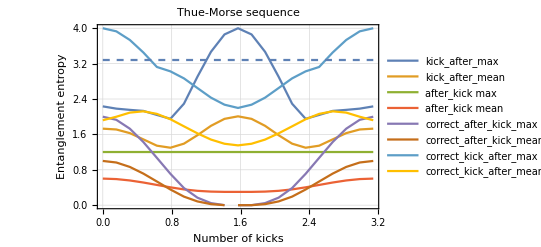

```mathematica
Show[ListLinePlot[{katmmax,katmmean,wtmmax,wtmmean,tmmax,tmmean,katcmmax,kactmmean},PlotTheme->"Detailed",PlotLegends->{"kick_after_max","kick_after_mean","after_kick max","after_kick mean","correct_after_kick_max","correct_after_kick_mean","correct_kick_after_max","correct_kick_after_mean"}],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},PlotLabel->HoldForm[Thue-Morse sequence],LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotRange->All]
```

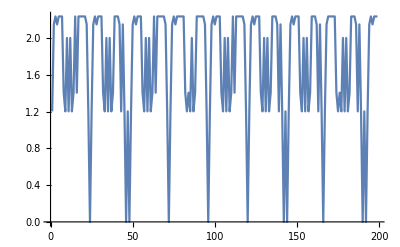

```mathematica
ListLinePlot[Drop[katmn[[1]],1]]
```

## Integrating TM sequence

```mathematica
TM=Table[(-1)^ThueMorse[i],{i,0,20000}];
```

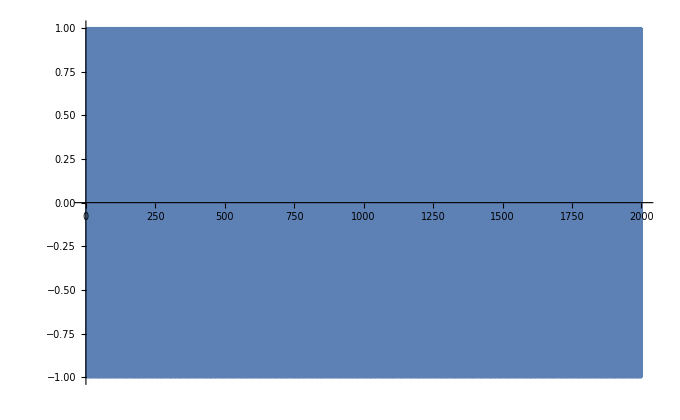

```mathematica
ListLinePlot[TM]
```

```mathematica
RS = Table[RudinShapiro[n],{n,1,20000}];
```

```mathematica
RS
```

{1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,19786,1,-1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1}
 |  |  |  |

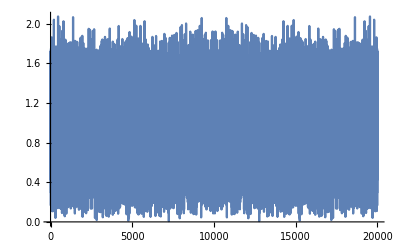

```mathematica
ListLinePlot[Abs[Fourier[RS]],PlotRange->All]
```

```mathematica
rsd = Table[0,{i,1,20001}];
rsd[[1]]=0;
For[i=2,i<20002, i++,rsd[[i]]=RS[[i-1]]+rsd[[i-1]]];
```

```mathematica
rsd
```

{0,1,2,1,2,3,2,3,4,5,6,5,4,3,4,3,4,5,6,5,6,7,6,7,6,5,4,5,6,7,6,7,8,9,10,9,10,11,10,11,12,13,14,13,12,11,12,11,10,9,8,9,8,7,8,7,8,9,10,9,8,7,8,7,8,9,10,9,10,11,10,11,12,13,14,13,12,11,12,11,12,13,14,13,19833,195,194,195,194,193,192,193,192,191,192,191,192,193,194,193,192,191,192,191,192,193,194,193,194,195,194,195,196,197,198,197,196,195,196,195,194,193,192,193,192,191,192,191,192,193,194,193,192,191,192,191,192,193,194,193,194,195,194,195,196,197,198,197,196,195,196,195,196,197,198,197,198,199,198,199,198,197,196,197,198,199,198,199,200}
 |  |  |  |

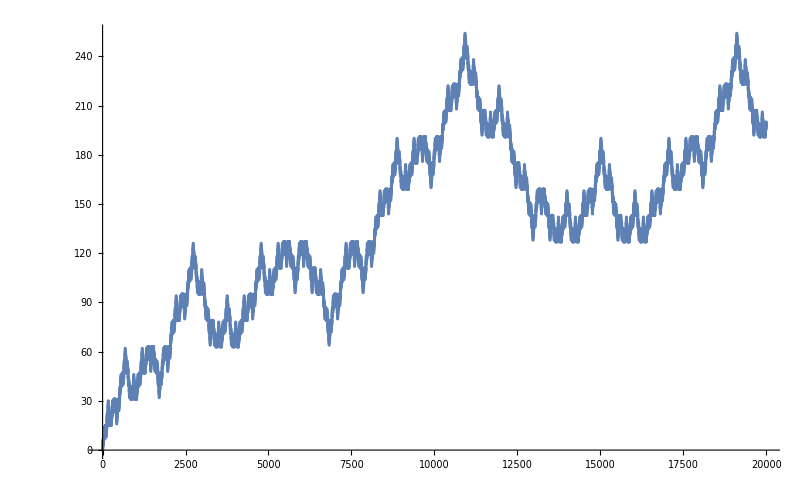

```mathematica
ListPlot[rsd]
```

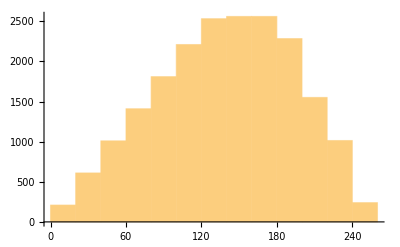

```mathematica
Histogram[rsd]
```

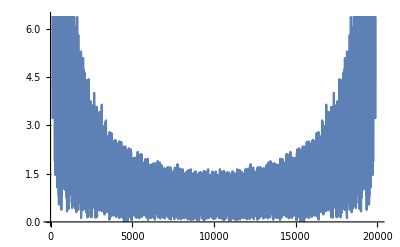

```mathematica
ListLinePlot[Abs[Fourier[rsd]]]
```

```mathematica
Fibo
```

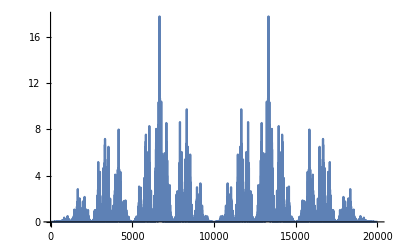

```mathematica
ListLinePlot[Abs[Fourier[TM]],PlotRange->All]
```

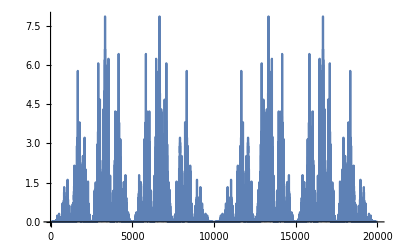

```mathematica
ListLinePlot[Abs[Fourier[20001/20002-tmd]],PlotRange->All]
```

```mathematica
rndom=Table[(-1)^RandomInteger[],{i,1,20000}];
```

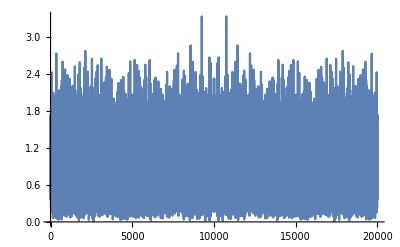

```mathematica
ListLinePlot[Abs[Fourier[rndom]]]
```

```mathematica
Mean[tmd]
```

20001/20002

```mathematica
tmd= Table[0,{i,1,20002}];
```

```mathematica
tmd[[1]] = 1
```

1

```mathematica
For[i=2,i<20002, i++,tmd[[i]]=TM[[i-1]]+tmd[[i-1]]]
```

```mathematica
tmd
```

{1,2,1,0,1,0,1,2,1,0,1,2,1,2,1,0,1,0,1,2,1,2,1,0,1,2,1,0,1,0,1,2,1,0,1,2,1,2,1,0,1,2,1,0,1,0,1,2,1,2,1,0,1,0,1,2,1,0,1,2,1,2,1,0,1,0,1,2,1,2,1,0,1,2,1,0,1,0,1,2,1,2,1,0,1,0,1,2,1,0,1,2,1,2,1,0,1,2,1,0,1,0,1,2,1,0,1,2,1,2,1,0,1,0,1,2,1,2,1,0,1,2,1,0,1,0,1,2,1,0,1,2,1,2,1,0,1,2,1,0,1,0,1,2,1,2,1,0,1,0,1,2,1,0,1,2,1,2,1,0,1,2,1,0,1,0,1,2,1,0,1,2,1,2,1,0,1,0,1,2,1,2,1,0,1,2,1,0,1,0,1,2,1,2,1,0,1,0,1,2,1,0}

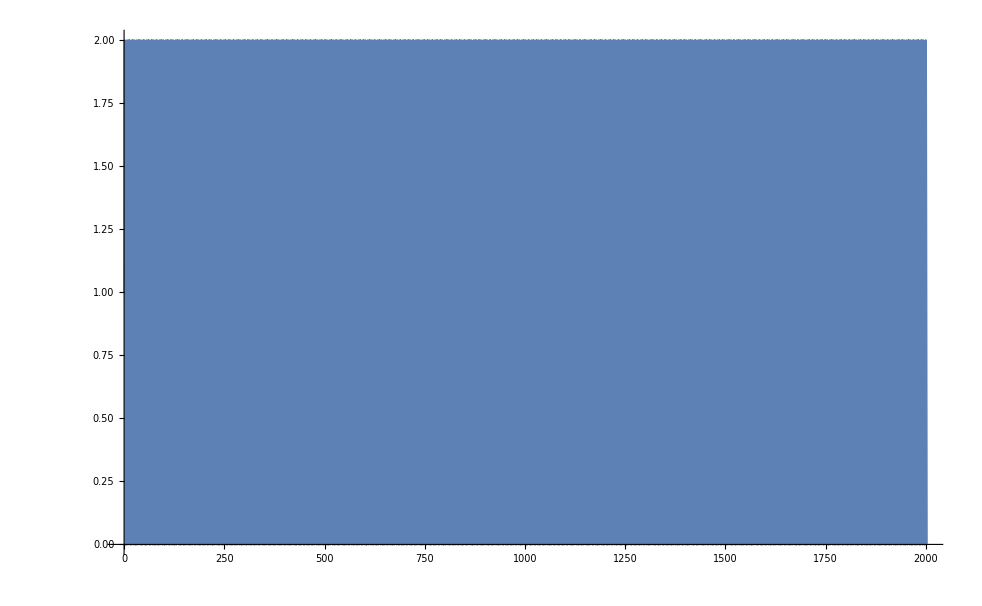

```mathematica
ListLinePlot[tmd]
```

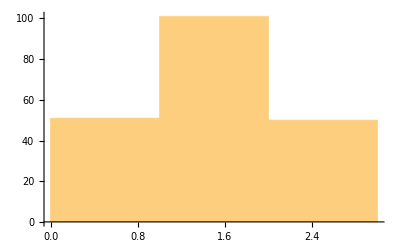

```mathematica
Histogram[tmd]
```

```mathematica
Fourier[TM]
```

{-0.0705346+0. ⅈ,-0.0704997+0.00221815 ⅈ,-0.0702971+0.00434418 ⅈ,-0.0705871+0.00787873 ⅈ,-0.0630062+0.0128906 ⅈ,-0.0677402+0.02065 ⅈ,-0.0669397+0.0110472 ⅈ,-0.0368099+0.0176012 ⅈ,-0.0508334+0.0629729 ⅈ,-0.140385-0.0593074 ⅈ,-0.177952+0.0871515 ⅈ,-0.0545772-0.0255406 ⅈ,-0.0259622+0.0167852 ⅈ,-0.0332987-0.00203849 ⅈ,-0.0262236+0.0816775 ⅈ,-0.450824+0.121435 ⅈ,0.000252928+0.440873 ⅈ,-0.174023-0.469699 ⅈ,0.242073-0.330449 ⅈ,-0.036515-0.0167579 ⅈ,-0.321343-0.410569 ⅈ,0.129968-0.682156 ⅈ,-0.373055+0.00901226 ⅈ,0.0557232+0.0986741 ⅈ,-0.167091+0.0134746 ⅈ,-0.188628-0.0112781 ⅈ,-0.177269+0.0175142 ⅈ,-0.155685+0.205875 ⅈ,-0.433-0.351743 ⅈ,-1.38217+0.446706 ⅈ,-0.557453-0.412117 ⅈ,0.13739+0.349092 ⅈ,-0.726085+0.746493 ⅈ,-0.633364-0.564059 ⅈ,2.24664+0.041981 ⅈ,0.356152-1.49462 ⅈ,0.207077+0.768805 ⅈ,-0.186054+0.390777 ⅈ,0.0346783+0.290529 ⅈ,-0.187175-0.106814 ⅈ,0.846074-1.18727 ⅈ,-0.920321-0.322177 ⅈ,1.23841+1.07322 ⅈ,0.0694352+1.03831 ⅈ,0.10399+0.112728 ⅈ,0.626219+0.247343 ⅈ,0.273171+0.580072 ⅈ,0.0854766-0.135776 ⅈ,-0.0808123+0.0647324 ⅈ,0.0162308+0.0457066 ⅈ,0.00403677+0.0663455 ⅈ,-0.00808571+0.0843117 ⅈ,0.00696586+0.129469 ⅈ,-0.217741+0.0993817 ⅈ,-0.278894+0.67267 ⅈ,-0.267437-0.0313969 ⅈ,0.4275+0.0631 ⅈ,0.097243+0.692078 ⅈ,-0.536759-0.364647 ⅈ,1.85894-1.86611 ⅈ,-0.906861-1.28407 ⅈ,1.05607+0.791889 ⅈ,0.218672+0.566263 ⅈ,0.346324+0.118457 ⅈ,-0.319526-0.198754 ⅈ,-0.269753-2.52224 ⅈ,-1.08435+1.17658 ⅈ,4.16154-0.122169 ⅈ,1.71882+1.63958 ⅈ,0.270056-0.340535 ⅈ,1.87155-1.00719 ⅈ,1.74574+0.70858 ⅈ,-0.946533-1.01901 ⅈ,-0.61444+0.472328 ⅈ,-0.142532-0.370409 ⅈ,-0.0665047-0.301989 ⅈ,-0.127698-0.246451 ⅈ,-0.324609-0.279359 ⅈ,0.603307-0.81198 ⅈ,-0.754588-1.70705 ⅈ,0.655973+0.293187 ⅈ,-0.612821+0.940969 ⅈ,-0.560256-0.239199 ⅈ,1.02903+0.463917 ⅈ,0.117033+2.88477 ⅈ,1.20884+0.0626347 ⅈ,-1.03178+0.0937893 ⅈ,-0.209086-0.106434 ⅈ,-0.0163019+0.151699 ⅈ,0.270512+0.0625572 ⅈ,0.6121+0.52894 ⅈ,-0.124283-0.343569 ⅈ,-0.569112+0.659883 ⅈ,-0.242537-0.0140527 ⅈ,0.124066+0.0659314 ⅈ,0.0354118+0.165276 ⅈ,0.000698827+0.0237569 ⅈ,0.133765-0.00542392 ⅈ,0.0747269-0.0118022 ⅈ,0.0738087+0.0039003 ⅈ,0.0707958+0.00113287 ⅈ,0.0707958-0.00113287 ⅈ,0.0738087-0.0039003 ⅈ,0.0747269+0.0118022 ⅈ,0.133765+0.00542392 ⅈ,0.000698827-0.0237569 ⅈ,0.0354118-0.165276 ⅈ,0.124066-0.0659314 ⅈ,-0.242537+0.0140527 ⅈ,-0.569112-0.659883 ⅈ,-0.124283+0.343569 ⅈ,0.6121-0.52894 ⅈ,0.270512-0.0625572 ⅈ,-0.0163019-0.151699 ⅈ,-0.209086+0.106434 ⅈ,-1.03178-0.0937893 ⅈ,1.20884-0.0626347 ⅈ,0.117033-2.88477 ⅈ,1.02903-0.463917 ⅈ,-0.560256+0.239199 ⅈ,-0.612821-0.940969 ⅈ,0.655973-0.293187 ⅈ,-0.754588+1.70705 ⅈ,0.603307+0.81198 ⅈ,-0.324609+0.279359 ⅈ,-0.127698+0.246451 ⅈ,-0.0665047+0.301989 ⅈ,-0.142532+0.370409 ⅈ,-0.61444-0.472328 ⅈ,-0.946533+1.01901 ⅈ,1.74574-0.70858 ⅈ,1.87155+1.00719 ⅈ,0.270056+0.340535 ⅈ,1.71882-1.63958 ⅈ,4.16154+0.122169 ⅈ,-1.08435-1.17658 ⅈ,-0.269753+2.52224 ⅈ,-0.319526+0.198754 ⅈ,0.346324-0.118457 ⅈ,0.218672-0.566263 ⅈ,1.05607-0.791889 ⅈ,-0.906861+1.28407 ⅈ,1.85894+1.86611 ⅈ,-0.536759+0.364647 ⅈ,0.097243-0.692078 ⅈ,0.4275-0.0631 ⅈ,-0.267437+0.0313969 ⅈ,-0.278894-0.67267 ⅈ,-0.217741-0.0993817 ⅈ,0.00696586-0.129469 ⅈ,-0.00808571-0.0843117 ⅈ,0.00403677-0.0663455 ⅈ,0.0162308-0.0457066 ⅈ,-0.0808123-0.0647324 ⅈ,0.0854766+0.135776 ⅈ,0.273171-0.580072 ⅈ,0.626219-0.247343 ⅈ,0.10399-0.112728 ⅈ,0.0694352-1.03831 ⅈ,1.23841-1.07322 ⅈ,-0.920321+0.322177 ⅈ,0.846074+1.18727 ⅈ,-0.187175+0.106814 ⅈ,0.0346783-0.290529 ⅈ,-0.186054-0.390777 ⅈ,0.207077-0.768805 ⅈ,0.356152+1.49462 ⅈ,2.24664-0.041981 ⅈ,-0.633364+0.564059 ⅈ,-0.726085-0.746493 ⅈ,0.13739-0.349092 ⅈ,-0.557453+0.412117 ⅈ,-1.38217-0.446706 ⅈ,-0.433+0.351743 ⅈ,-0.155685-0.205875 ⅈ,-0.177269-0.0175142 ⅈ,-0.188628+0.0112781 ⅈ,-0.167091-0.0134746 ⅈ,0.0557232-0.0986741 ⅈ,-0.373055-0.00901226 ⅈ,0.129968+0.682156 ⅈ,-0.321343+0.410569 ⅈ,-0.036515+0.0167579 ⅈ,0.242073+0.330449 ⅈ,-0.174023+0.469699 ⅈ,0.000252928-0.440873 ⅈ,-0.450824-0.121435 ⅈ,-0.0262236-0.0816775 ⅈ,-0.0332987+0.00203849 ⅈ,-0.0259622-0.0167852 ⅈ,-0.0545772+0.0255406 ⅈ,-0.177952-0.0871515 ⅈ,-0.140385+0.0593074 ⅈ,-0.0508334-0.0629729 ⅈ,-0.0368099-0.0176012 ⅈ,-0.0669397-0.0110472 ⅈ,-0.0677402-0.02065 ⅈ,-0.0630062-0.0128906 ⅈ,-0.0705871-0.00787873 ⅈ,-0.0702971-0.00434418 ⅈ,-0.0704997-0.00221815 ⅈ}